## Quantum (theory work)

P(τ_2,τ_3)=(i^3((2πℏ ω_F)/V))^3 π^2/(|aa'|)^2Exp[-2 σ_F^2(((3+4 σ_F^4(B_2^2+B_2 B_3+B_3^2))τ_2^2+(3+4 σ_F^4(B_1(B_2-B_3)+B_2(2 B_2+B_3)))τ_2 τ_3+(3+4 σ_F^4(B_2^2+B_2 B_1+B_1^2))τ_3^2)/(9+8σ_F^4[2(B_1^2+B_2^2+B_3^2)+B_1 B_2+B_2 B_3+B_3 B_1]+16 σ_F^8(B_1 B_2+B_2 B_3+B_3 B_1)^2))]
a=1/σF^2-ⅈ(B2+B3);
aprime=1/σF^2-ⅈ(B1+B3)-1/(4a)(1/σF^2-2ⅈB3)^2;
bprime=-ⅈ(A1-A3+t+τ-2/(4a)(1/σF^2-2ⅈB3)(A2-A3+τ));
cprime=1/(4a)(A2-A3+τ)^2+ⅈ ω0/3(2t+τ);
cnprime=cn((2πℏωF)/V)^(3/2)ⅇ^(ⅈ(Kf1+Kf2+Kf3-ω0t))√(π^2/aaprime);
Normalization:(π^2/Abs[(1/σFtest^2-ⅈ(B[2]+B[3]))(1/σFtest^2-ⅈ(B[1]+B[3])-(1/(4(1/σFtest^2-ⅈ(B[2]+B[3]))))(1/σFtest^2-2ⅈ(B[3]))^2)])

## Quantum (code) (Analytical solution, approximated with narrowband filters)

```mathematica
Quantum[σF_,t_,τ_,A1_,A2_,A3_,B1_,B2_,B3_]:=(π^2/Abs[(1/σFtest^2-ⅈ(B[2]+B[3]))(1/σFtest^2-ⅈ(B[1]+B[3])-(1/(4(1/σFtest^2-ⅈ(B[2]+B[3]))))(1/σFtest^2-2ⅈ(B[3]))^2)])ⅇ^((2 σF^2 (-3 A3^2-4 A3^2 B1^2 σF^4-4 A3^2 B1 B2 σF^4-4 A3^2 B2^2 σF^4+A2^2 (-3-4 (B1^2+B1 B3+B3^2) σF^4)+A1^2 (-3-4 (B2^2+B2 B3+B3^2) σF^4)+3 A3 t+4 A3 B1 B2 σF^4 t+8 A3 B2^2 σF^4 t-4 A3 B1 B3 σF^4 t+4 A3 B2 B3 σF^4 t-3 t^2-4 B2^2 σF^4 t^2-4 B2 B3 σF^4 t^2-4 B3^2 σF^4 t^2+(6 A3+8 A3 (B1^2+B1 B2+B2^2) σF^4-(3+4 (B1 (B2-B3)+B2 (2 B2+B3)) σF^4) t) τ-(3+4 (B1^2+B1 B2+B2^2) σF^4) τ^2+A1 (A2 (3+4 (B1 (-B2+B3)+B3 (B2+2 B3)) σF^4)+3 (A3-2 t-τ)+4 σF^4 (A3 B1 (B2-B3)+A3 B2 (2 B2+B3)-2 B2 B3 t-B2 (B1+B3) τ-2 B2^2 (t+τ)+B3 (-2 B3 t+B1 τ)))+A2 (A3 (3+4 (2 B1^2-B2 B3+B1 (B2+B3)) σF^4)+3 (t-τ)+4 σF^4 (-2 B1^2 τ+B3 (2 B3 t+B2 (t+τ))-B1 (B3 (-t+τ)+B2 (t+τ))))))/(9+8 (2 B1^2+2 B2^2+B2 B3+2 B3^2+B1 (B2+B3)) σF^4+16 (B2 B3+B1 (B2+B3))^2 σF^8));
```

## Classical (theory work)

a_i^2 =1/(2 σF^2)-ⅈ B_i; 
E1 = E0/(2 √π a1)Exp[-((A1-t1)^2(1/(2 σF^2)+ⅈ B1))/(4((1/(2 σF^2))^2+B1^2))];
E2=E0/(2 √π a2)Exp[-((A2-(t1+t))^2(1/(2 σF^2) +ⅈ B2))/(4((1/(2 σF^2))^2+B2^2))];
E3=E0/(2 √π a3)Exp[-((A3-(t1+t+τ))^2(1/(2 σF^2) +ⅈ B3))/(4((1/(2 σF^2))^2+B3^2))];
I1 = E0^2/((2 √π)^2((1/(2 σF^2))^2+ B1^2))ⅇ^(-(A1-t1)^2/(2(((1/(2 σF^2))^2+B1^2)/(1/(2 σF^2)))));
I2 = E0^2/((2 √π)^2((1/(2 σF^2))^2+ B2^2))ⅇ^(-(A2-(t1+t))^2/(2(((1/(2 σF^2))^2+B2^2)/(1/(2 σF^2)))));
I3 = E0^2/((2 √π)^2((1/(2 σF^2))^2+ B3^2))ⅇ^(-(A3-(t1+t+τ))^2/(2(((1/(2 σF^2))^2+B3^2)/(1/(2 σF^2)))));
P[t_,τ_]=(η E0^6)/((2 √π)^6((1/(2 σF^2))^2+ B1^2)((1/(2 σF^2))^2+ B2^2)((1/(2 σF^2))^2+ B3^2))∫_(-∞)^∞ ⅇ^(-(A1-t1)^2/(2(((1/(2 σF^2))^2+B1^2)/(1/(2 σF^2)))))ⅇ^(-(A2-(t1+t))^2/(2(((1/(2 σF^2))^2+B2^2)/(1/(2 σF^2)))))ⅇ^(-(A3-(t1+t+τ))^2/(2(((1/(2 σF^2))^2+B3^2)/(1/(2 σF^2)))))ⅆt1

```mathematica
SimplifiedP=(ⅇ^(-(2 σF^2 (A3^2-A3 t+t^2+2 A3^2 B1^2 σF^4+2 A3^2 B2^2 σF^4-4 A3 B2^2 t σF^4+2 B2^2 t^2 σF^4+2 B3^2 t^2 σF^4+A2^2 (1+2 (B1^2+B3^2) σF^4)+A1^2 (1+2 (B2^2+B3^2) σF^4)+(-2 A3+t-4 A3 (B1^2+B2^2) σF^4+4 B2^2 t σF^4) τ+(1+2 (B1^2+B2^2) σF^4) τ^2-A2 (A3+t+4 A3 B1^2 σF^4-τ+4 σF^4 (B3^2 t-B1^2 τ))+A1 (2 t-A3 (1+4 B2^2 σF^4)-A2 (1+4 B3^2 σF^4)+τ+4 σF^4 (B3^2 t+B2^2 (t+τ)))))/(3+8 σF^4 (B1^2+B2^2+B3^2+2 (B2^2 B3^2+B1^2 (B2^2+B3^2)) σF^4))) E0^6 η σF^11)/(π^(5/2) √((1+4 B1^2 σF^4) (1+4 B2^2 σF^4) (1+4 B3^2 σF^4) (3+8 σF^4 (B1^2+B2^2+B3^2+2 (B2^2 B3^2+B1^2 (B2^2+B3^2)) σF^4))))
```

## Classical (code)

```mathematica
Classical[σF_,t_,τ_,A1_,A2_,A3_,B1_,B2_,B3_]:=ⅇ^(-(2 σF^2 (A3^2-A3 t+t^2+2 A3^2 B1^2 σF^4+2 A3^2 B2^2 σF^4-4 A3 B2^2 t σF^4+2 B2^2 t^2 σF^4+2 B3^2 t^2 σF^4+A2^2 (1+2 (B1^2+B3^2) σF^4)+A1^2 (1+2 (B2^2+B3^2) σF^4)+(-2 A3+t-4 A3 (B1^2+B2^2) σF^4+4 B2^2 t σF^4) τ+(1+2 (B1^2+B2^2) σF^4) τ^2-A2 (A3+t+4 A3 B1^2 σF^4-τ+4 σF^4 (B3^2 t-B1^2 τ))+A1 (2 t-A3 (1+4 B2^2 σF^4)-A2 (1+4 B3^2 σF^4)+τ+4 σF^4 (B3^2 t+B2^2 (t+τ)))))/(3+8 σF^4 (B1^2+B2^2+B3^2+2 (B2^2 B3^2+B1^2 (B2^2+B3^2)) σF^4)));
```

## Analyzing variances of the quantum and the classical results

### Using ,⟨tτ⟩ for comparison

```mathematica
norm=∫_(-∞)^∞ ∫_(-∞)^∞ Classical[0.1,t,τ,0,0,0,B1,B2,B3]ⅆtⅆτ
```

```mathematica
norm1[B1_,B2_,B3_]:=(471.23889803846896+0.1256637061435917 B3^2+B2^2 (0.1256637061435917+0.000025132741228718343 B3^2)+B1^2 (0.1256637061435917+0.000025132741228718343 B2^2+0.000025132741228718343 B3^2))/(√(0.75+0.0002000000000000001 B3^2+B2^2 (0.0002000000000000001+4.0000000000000034*^-8 B3^2)+B1^2 (0.0002000000000000001+4.0000000000000034*^-8 B2^2+4.0000000000000034*^-8 B3^2)))
```

```mathematica
res=∫_(-∞)^∞ ∫_(-∞)^∞ t τ Classical[0.1,t,τ,0,0,0,B1,B2,B3]ⅆtⅆτ
```

#### Quantum case

We are calculating Norm=∫∫P_quantum(t,τ)ⅆtⅆτ

```mathematica
∫_(-∞)^∞ ∫_(-∞)^∞ Quantum[0.1,t,τ,0,0,0,B1,B2,B3]ⅆtⅆτ
```

$Aborted

Now, we are calculating =∫∫tτP_quantum(t,τ)ⅆtⅆτ

```mathematica
∫_(-∞)^∞ ∫_(-∞)^∞ t τ ⅇ^(numer[0.1,t,τ,0,0,0,B1,B2,B3]/denom[0.1,t,τ,0,0,0,B1,B2,B3])ⅆtⅆτ
```

Taking the ratio gives ⟨tτ⟩ := qCov

```mathematica
qCov[B1_,B2_,B3_]:=(1/(3.7486824790711176*^11+6.664324407237545*^7 B3^2+B2^4 (17771.531752633462+1.7771531752633467 B3^2)+B2^2 (1.6660811018093863*^8+28878.73909802937 B3^2)+B2^3 (17771.531752633462 B3+0.8885765876316734 B3^3)+B2 (8.330405509046932*^7 B3+8885.765876316731 B3^3)+B1^3 (0.8885765876316734 B2^3-8885.765876316731 B3+0.8885765876316734 B2^2 B3-0.8885765876316734 B3^3+B2 (8885.765876316731-0.8885765876316734 B3^2))+B1^2 (6.664324407237545*^7+1.7771531752633467 B2^4+6.220036113421713 B2^3 B3+2221.4414690791823 B3^2+B2^2 (28878.73909802937+3.5543063505266934 B3^2)+B2 (22214.414690791826 B3-0.8885765876316734 B3^3))+B1 (-1.666081101809387*^7 B3+3.5543063505266934 B2^4 B3-8885.765876316731 B3^3+B2^3 (17771.531752633462+6.220036113421713 B3^2)+B2 (8.330405509046932*^7+22214.414690791826 B3^2)+B2^2 (22214.414690791826 B3+0.8885765876316734 B3^3)))/(2 √((23561.944901923438+3.141592653589793 B2^2+3.141592653589793 B2 B3+3.141592653589793 B3^2)/(5.6249999999999955*^7+4999.999999999998 B2 B3+9999.999999999996 B3^2+B2^2 (9999.999999999996+1. B3^2)+B1^2 (9999.999999999996+1. B2^2+2. B2 B3+1. B3^2)+B1 (4999.999999999998 B3+2. B2^2 B3+B2 (4999.999999999998+2. B3^2)))) √((6.714349161689327*^8-2.2617277734851675*^-15 B2^4+59683.10365946071 B2 B3-2.2617277734851675*^-15 B2^3 B3+119366.20731892143 B3^2+B2^2 (119366.20731892141+11.936620731892146 B3^2)+B1^2 (119366.20731892143+11.936620731892146 B2^2+23.873241463784296 B2 B3+11.936620731892146 B3^2)+B1 (-2.2617277734851675*^-15 B2^3+59683.103659460736 B3+23.873241463784296 B2^2 B3+B2 (59683.10365946071+23.873241463784296 B3^2)))/((7499.999999999997+1. B2^2+1. B2 B3+1. B3^2) (5.6249999999999955*^7+4999.999999999998 B2 B3+9999.999999999996 B3^2+B2^2 (9999.999999999996+1. B3^2)+B1^2 (9999.999999999996+1. B2^2+2. B2 B3+1. B3^2)+B1 (4999.999999999998 B3+2. B2^2 B3+B2 (4999.999999999998+2. B3^2))))) (4.2187499999999945*^11+7.499999999999994*^7 B3^2+B2^4 (19999.999999999993+2. B3^2)+B2^2 (1.8749999999999982*^8+32499.999999999985 B3^2)+B2^3 (19999.999999999993 B3+1. B3^3)+B2 (9.374999999999991*^7 B3+9999.999999999996 B3^3)+B1^3 (1. B2^3-9999.999999999996 B3+1. B2^2 B3-1. B3^3+B2 (9999.999999999996-1. B3^2))+B1^2 (7.499999999999994*^7+2. B2^4+7. B2^3 B3+2499.999999999998 B3^2+B2^2 (32499.999999999985+4. B3^2)+B2 (24999.99999999999 B3-1. B3^3))+B1 (-1.875*^7 B3+4. B2^4 B3-9999.999999999996 B3^3+B2^3 (19999.999999999993+7. B3^2)+B2 (9.374999999999991*^7+24999.99999999999 B3^2)+B2^2 (24999.999999999985 B3+1. B3^3)))))(-((0.00048367983046245834 (4.218749999999996*^11+8. B2^6+1.6874999999999985*^8 B2 B3+12.000000000000002 B2^5 B3+B2^4 (89999.99999999997+6.000000000000001 B3^2)+B2^2 (3.374999999999997*^8+22499.999999999993 B3^2)+B1^3 (1. B2^3-3.0000000000000004 B2^2 B3+3.0000000000000004 B2 B3^2-1. B3^3)+B2^3 (89999.99999999997 B3+1. B3^3)+B1^2 (22499.999999999993 B2^2+6.000000000000001 B2^4-44999.999999999985 B2 B3-9. B2^3 B3+22499.999999999993 B3^2+3.0000000000000004 B2 B3^3)+B1 (12.000000000000002 B2^5-1.6874999999999985*^8 B3+B2 (1.6874999999999985*^8-44999.999999999985 B3^2)+B2^3 (89999.99999999997-9. B3^2)+B2^2 (-44999.999999999985 B3-3.0000000000000004 B3^3))))/((7499.999999999997+1. B1 B2+2. B2^2-1. B1 B3+1. B2 B3)^2 (7499.999999999997+1. B2^2+1. B2 B3+1. B3^2) √((7499.999999999997+1. B2^2+1. B2 B3+1. B3^2)/(5.6249999999999955*^7+4999.999999999998 B2 B3+9999.999999999996 B3^2+B2^2 (9999.999999999996+1. B3^2)+B1^2 (9999.999999999996+1. B2^2+2. B2 B3+1. B3^2)+B1 (4999.999999999998 B3+2. B2^2 B3+B2 (4999.999999999998+2. B3^2)))) ((5.6249999999999955*^7-1.894780628693601*^-16 B2^4+4999.999999999998 B2 B3-1.894780628693601*^-16 B2^3 B3+9999.999999999998 B3^2+B2^2 (9999.999999999996+1. B3^2)+B1^2 (9999.999999999998+1. B2^2+2.0000000000000004 B2 B3+1. B3^2)+B1 (-1.894780628693601*^-16 B2^3+5000. B3+2.0000000000000004 B2^2 B3+B2 (4999.999999999998+2.0000000000000004 B3^2)))/((7499.999999999997+1. B2^2+1. B2 B3+1. B3^2) (5.6249999999999955*^7+4999.999999999998 B2 B3+9999.999999999996 B3^2+B2^2 (9999.999999999996+1. B3^2)+B1^2 (9999.999999999996+1. B2^2+2. B2 B3+1. B3^2)+B1 (4999.999999999998 B3+2. B2^2 B3+B2 (4999.999999999998+2. B3^2)))))^(3/2))));
```

#### Classical case

```mathematica
cCov[B1_,B2_,B3_]:=-((0.0044546623974653695 (1.5624999999999975*^10+1.874999999999998*^7 B2^2+7499.999999999995 B2^4+1. B2^6) (1.8749999999999985*^7+4999.999999999998 B3^2+B2^2 (4999.999999999998+1. B3^2)+B1^2 (4999.999999999998+1. B2^2+1. B3^2))^2)/((2499.999999999999+1. B2^2)^2 (1.8749999999999985*^7-1.421085471520201*^-16 B2^4+4999.999999999998 B3^2+B2^2 (4999.999999999996+1. B3^2)+B1^2 (4999.999999999998+1. B2^2+1. B3^2)) √(5.8904862254808575*^7-4.46447167745105*^-16 B2^4+15707.96326794896 B3^2+B2^2 (15707.963267948955+3.141592653589793 B3^2)+B1^2 (15707.96326794896+3.141592653589793 B2^2+3.141592653589793 B3^2))))/((471.23889803846896+0.1256637061435917 B3^2+B2^2 (0.1256637061435917+0.000025132741228718343 B3^2)+B1^2 (0.1256637061435917+0.000025132741228718343 B2^2+0.000025132741228718343 B3^2))/(√(0.75+0.0002000000000000001 B3^2+B2^2 (0.0002000000000000001+4.0000000000000034*^-8 B3^2)+B1^2 (0.0002000000000000001+4.0000000000000034*^-8 B2^2+4.0000000000000034*^-8 B3^2))))
```

#### Comparing results

```mathematica
cCov[10,-20,-30]
```

-58.

```mathematica
qCov[100,-200,-300]
```

-1050.

```mathematica
FindArgMin[Abs[qCov[10,-20,z]],z]
```

FindArgMin::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

{270.012}

### Using SVD for comparison

#### For σF=0.1, B1=10, B2=20,B3=30,Range=50

```mathematica
σFtest=0.5;
B[1]=10;
B[2]=20;
B[3]=30;
range=50;
clas=Table[N[Classical[σFtest,t-range -1,τ-range -1,A[1],A[2],A[3],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
clas=clas/Total[Total[clas]];
quan=Table[N[Quantum[σFtest,t-range -1,τ-range -1,A[1],A[2],A[3],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
quan=quan/Total[Total[quan]];
```

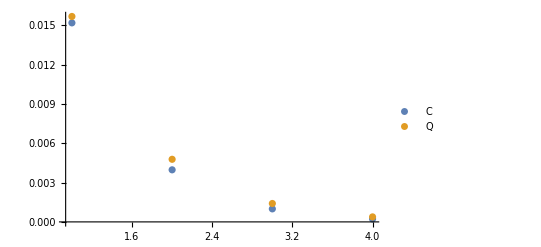

```mathematica
{uc,wc,vc}=SingularValueDecomposition[clas];
{uq,wq,vq}=SingularValueDecomposition[quan];
ListPlot[{Part[Diagonal[wc],1;;4],Part[Diagonal[wq],1;;4]},PlotLegends-> {"C","Q"},PlotRange->All]
```

```mathematica
plot1=ListContourPlot[uq.wq.DiagonalMatrix[{1,1},0,Dimensions[wq][[1]]].vq†,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->10,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"quantum",PlotRange->Full,Contours->5,ImageSize->Scaled[0.25]];
plot2=ListContourPlot[uc.wc.DiagonalMatrix[{1,1},0,Dimensions[wc][[1]]].vc†,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->10,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"classical",PlotRange->Full,Contours->5,ImageSize->Scaled[0.25]];
GraphicsRow[{plot1,plot2},ImageSize->Scaled[0.25]]
```

-Graphics-

## Plots

We map all the results from analytical as well numerical solutions into matrices of dimension (2 range+1)x(2 range +1) where x and y axis in the plots go from (-range, range).

```mathematica
Do[KF[i]=0,{i,1,3}];
Do[A[i]=0,{i,1,3}];
```

### Experiment 0

```mathematica
range=50;
σFtest=0.5;
B[1]=12.5*2;
B[2]=-12.5;
B[3]-12.5;
classical0=Table[N[Classical[σFtest,t-range -1,τ-t,A[1],A[2],A[3],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
classical0=classical0/Total[Total[classical0]];
quanalytical0=Table[N[Quantum[0.1,t-range -1,τ-t,0,0,0,B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
quanalytical0=quanalytical0/Total[Total[quanalytical0]];
plot1=ListContourPlot[classical0,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->10,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"classical",PlotRange->Full,Contours-> 5,ImageSize->Scaled[1]];
plot2=ListContourPlot[quanalytical0,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->10,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"quantum",PlotRange->Full,Contours-> 5,ImageSize->Scaled[1]];
GraphicsRow[{plot2,plot1}]
```

$Aborted

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of quanalytical0/Total[Total[quanalytical0]].

```mathematica
ratioτ=quanalytical0[[0+range+1,1+range+1]]/classical0[[0+range+1,1+range+1]]
```

0.97709

```mathematica
ratiot=classical0[[1+range+1,0+range+1]]/quanalytical0[[1+range+1,0+range+1]]
```

0.977398

### Experiment 1: Range = -10, 10, B1=10, B2=-20, B3=-30,σF =0.5

```mathematica
range=10;
B[1]=10;
B[2]=20;
B[3]=30;
σFtest=0.5;
```

Classical

```mathematica
classical1=Table[N[Classical[σFtest,t-range -1,τ-range -1,A[1],A[2],A[3],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
classical1=classical1/Total[Total[classical1]];
```

Quantum (analytical solution)

```mathematica
quanalytical1=Table[N[Quantum[σFtest,t-range -1,τ-range -1,A[1],A[2],A[2],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
quanalytical1=quanalytical1/Total[Total[quanalytical1]];
```

For Quantum (numerical solution), we directly create the matrix. This is time consuming so we use get values in upper half and simply use those results in the lower half after inversion along the y-axis. We only do this because the plots are symmetrical.  
The code outputs the current value of (t,τ) at which the function is being calculated.

```mathematica
Do[k[i][ω_,ωF_]=KF[i]+A[i] (ω-ωF)+B[i] (ω-ωF)^2,{i,1,3}]
f[ω_,ωF_,σF_]=Exp[-(ω-ωF)^2/(2 σF^2)];
ClearAll[int2,result2]
Do[
Do[
int2[t,τ][ω1_,ω2_,ω3_,t1_,ωF_,σF_]=f[ω1,ωF,σF]*f[ω2,ωF,σF]*f[ω3,ωF,σF]*Exp[ⅈ (k[1][ω1,ωF]+k[2][ω2,ωF]+k[3][ω3,ωF]-ω1 t1 -ω2 (t1+t)-ω3 (t1+t+τ))],
{t,-range,range,1}
],{τ,-range,range,1}
]
Monitor[Do[
Do[
result2[t,τ]=NIntegrate[int2[t,τ][1/3+ϵ,1/3+δ,1/3-ϵ-δ,0,1/3,σFtest],{ϵ,-1/3,2/3},{δ,-1/3,2/3-ϵ}];result2[-t,-τ]=result2[t,τ]
,{t,-range,range,1}],{τ,0,range,1}],{t,τ}]
qunumerical1=Table[Abs[result2[t-range -1,τ-range -1]]^2,{t,1,2 range +1},{τ,1,2 range +1}];
qunumerical1 = qunumerical1/Total[Total[qunumerical1]];
```

Plotting

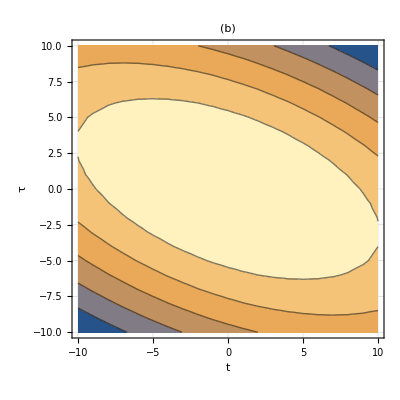

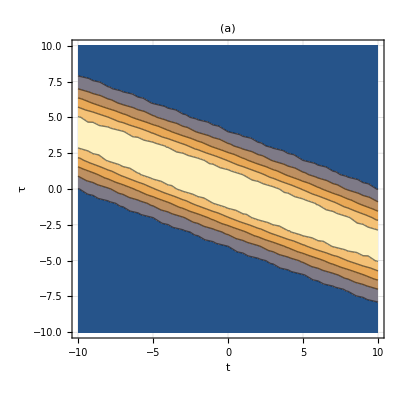

```mathematica
ListContourPlot[classical1,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(b)",PlotRange->Full,Contours-> 5,ImageSize->Scaled[0.5]]
ListContourPlot[quanalytical1,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(a)",PlotRange->Full,Contours->5,ImageSize->Scaled[0.5]]
```

```mathematica
ListContourPlot[qunumerical1,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True,PlotRange->Full,Contours->5,ImageSize->Scaled[0.5]]
```

-Graphics-

### Experiment 2: Range = -10, 10, B1=10, B2=+20, B3=+30,σF =0.5

```mathematica
range=50;
B[1]=25;
B[2]=-12.5;
B[3]=-12.5;
σFtest=0.5;
```

Classical

```mathematica
classical2=Table[N[Classical[σFtest,t-range -1,τ-range -1,A[1],A[2],A[3],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
classical2=classical2/Total[Total[classical2]];
```

Quantum (analytical solution)

```mathematica
quanalytical2=Table[N[Quantum[σFtest,t-range -1,τ-range -1,A[1],A[2],A[2],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
quanalytical2=quanalytical2/Total[Total[quanalytical2]];
```

For Quantum (numerical solution), we directly create the matrix. This is time consuming so we use get values in upper half and simply use those results in the lower half after inversion along the y-axis. We only do this because the plots are symmetrical.  
The code outputs the current value of (t,τ) at which the function is being calculated.

```mathematica
Do[k[i][ω_,ωF_]=KF[i]+A[i] (ω-ωF)+B[i] (ω-ωF)^2,{i,1,3}]
f[ω_,ωF_,σF_]=Exp[-(ω-ωF)^2/(2 σF^2)];
ClearAll[int2,result2]
Do[
Do[
int2[t,τ][ω1_,ω2_,ω3_,t1_,ωF_,σF_]=f[ω1,ωF,σF]*f[ω2,ωF,σF]*f[ω3,ωF,σF]*Exp[ⅈ (k[1][ω1,ωF]+k[2][ω2,ωF]+k[3][ω3,ωF]-ω1 t1 -ω2 (t1+t)-ω3 (t1+t+τ))],
{t,-range,range,1}
],{τ,-range,range,1}
]
Monitor[Do[
Do[
result2[t,τ]=NIntegrate[int2[t,τ][1/3+ϵ,1/3+δ,1/3-ϵ-δ,0,1/3,σFtest],{ϵ,-1/3,2/3},{δ,-1/3,2/3-ϵ}];result2[-t,-τ]=result2[t,τ]
,{t,-range,range,1}],{τ,0,range,1}],{t,τ}]
qunumerical2=Table[Abs[result2[t-range -1,τ-range -1]]^2,{t,1,2 range +1},{τ,1,2 range +1}];
qunumerical2= qunumerical2/Total[Total[qunumerical2]];
```

Plotting

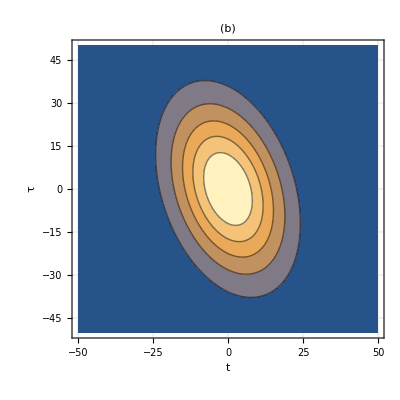

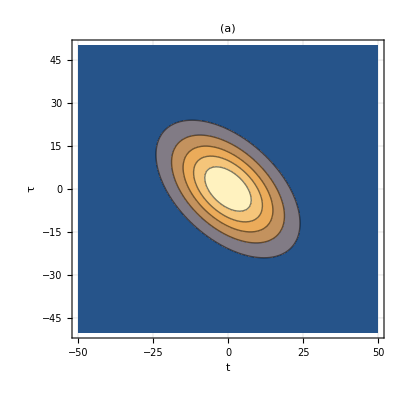

```mathematica
ListContourPlot[classical2,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(b)",PlotRange->Full,Contours-> 5,ImageSize->Scaled[0.5]]
ListContourPlot[quanalytical2,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(a)",PlotRange->Full,Contours->5,ImageSize->Scaled[0.5]]
```

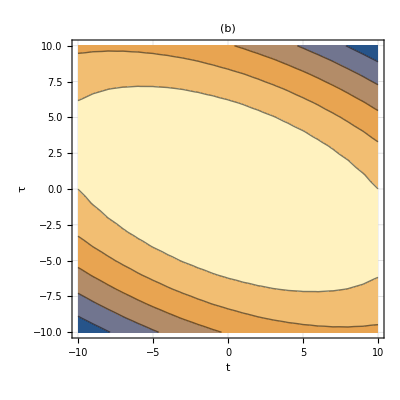

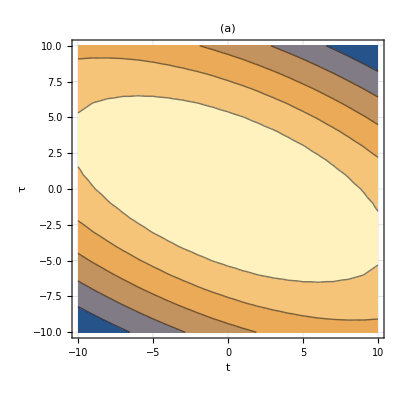

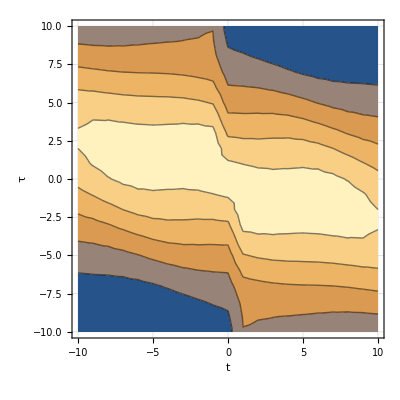

```mathematica
ListContourPlot[qunumerical2,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True,PlotRange->Full,Contours->5,ImageSize->Scaled[0.5]]
```

### Experiment 3: Range = (-50, 50), B1=10, B2=-20, B3=-30,σF =0.1

```mathematica
range=50;
B[1]=10;
B[2]=-20;
B[3]=-30;
σFtest=0.1;
```

Classical

```mathematica
classical3=Table[N[Classical[σFtest,t-range -1,τ-range -1,A[1],A[2],A[3],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
classical3=classical3/Total[Total[classical3]];
```

Quantum (analytical solution)

```mathematica
quanalytical3=Table[N[Quantum[σFtest,t-range -1,τ-range -1,A[1],A[2],A[2],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
quanalytical3=quanalytical3/Total[Total[quanalytical3]];
```

Plotting

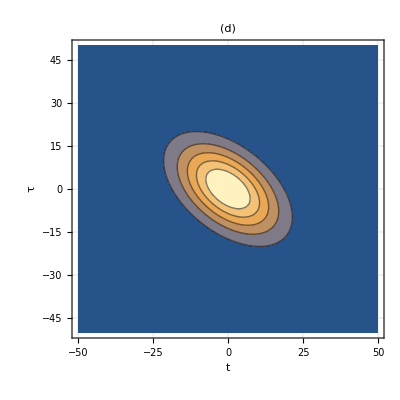

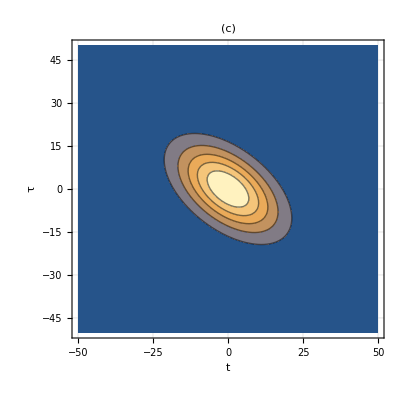

```mathematica
ListContourPlot[classical3,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(d)",PlotRange->Full,Contours-> 5,ImageSize->Scaled[0.5]]
ListContourPlot[quanalytical3,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(c)",PlotRange->Full,Contours->5,ImageSize->Scaled[0.5]]
```

### Experiment 4: Range = (-50, 50), B1=10, B2=+20, B3=+30,σF =0.1

```mathematica
range=50;
B[1]=10;
B[2]=20;
B[3]=30;
σFtest=0.1;
```

Classical

```mathematica
classical4=Table[N[Classical[σFtest,t-range -1,τ-range -1,A[1],A[2],A[3],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
classical4=classical4/Total[Total[classical4]];
```

Quantum (analytical solution)

```mathematica
quanalytical4=(π^2/Abs[(1/σFtest^2-ⅈ (B[2]+B[3])) (1/σFtest^2-ⅈ (B[1]+B[3])-(1/(4(1/σFtest^2-ⅈ (B[2]+B[3]))))(1/σFtest^2-2ⅈ (B[3]))^2)])Table[N[Exp[numer[σFtest,t-range -1,τ-range -1,A[1],A[2],A[3],B[1],B[2],B[3]]/denom[σFtest,t-range -1,τ-range -1,A[1],A[2],A[3],B[1],B[2],B[3]]]],{t,1,2 range +1},{τ,1,2 range +1}];
quanalytical4=quanalytical4/Total[Total[quanalytical4]];
```

Plotting

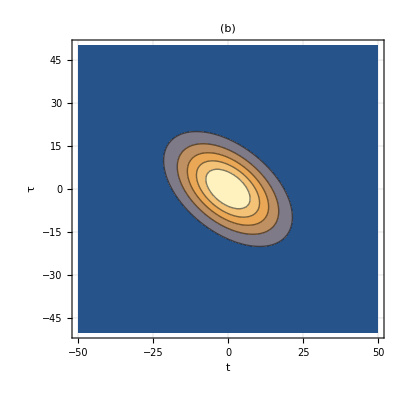

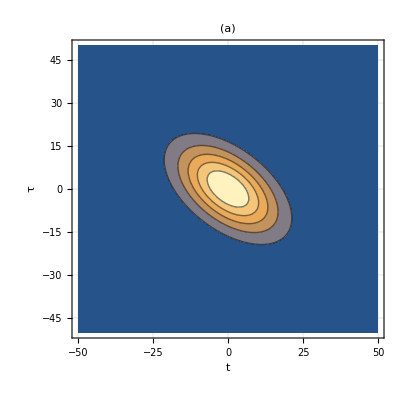

```mathematica
ListContourPlot[classical4,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(b)",PlotRange->Full,Contours-> 5,ImageSize->Scaled[0.5]]
ListContourPlot[quanalytical4,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(a)",PlotRange->Full,Contours->5,ImageSize->Scaled[0.5]]
```

### Experiment 5: Range = (-50, 50), B1=10, B2=-20, B3=-30,σF =0.5

```mathematica
ClearAll[classical5,quanalytical5,range,σFtest,B]
range=50;
B[1]=10;
B[2]=-20;
B[3]=-30;
σFtest=0.5;
```

Classical

```mathematica
classical5=Table[N[Classical[σFtest,t-range -1,τ-range -1,A[1],A[2],A[3],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
classical5=classical5/Total[Total[classical5]];
```

Quantum (analytical solution)

```mathematica
quanalytical5=Table[N[Quantum[σFtest,t-range -1,τ-range -1,A[1],A[2],A[2],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
quanalytical5=quanalytical5/Total[Total[quanalytical5]];
```

Plotting

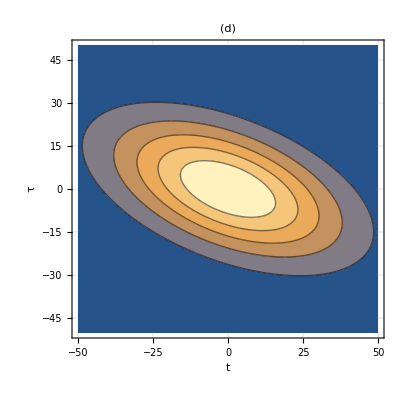

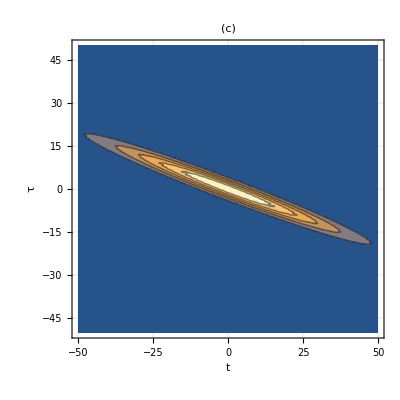

```mathematica
ListContourPlot[classical5,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(d)",PlotRange->Full,Contours-> 5,ImageSize->Scaled[0.5]]
ListContourPlot[quanalytical5,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(c)",PlotRange->Full,Contours->5,ImageSize->Scaled[0.5]]
```

### Experiment 6: Range = (-50, 50), B1=10, B2=20, B3=30,σF =0.5

```mathematica
range=50;
B[1]=10;
B[2]=20;
B[3]=30;
σFtest=0.5;
```

Classical

```mathematica
classical6=Table[N[Classical[σFtest,t-range -1,τ-range -1,A[1],A[2],A[3],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
classical6=classical6/Total[Total[classical6]];
```

Quantum (analytical solution)

```mathematica
quanalytical6=Table[N[Quantum[σFtest,t-range -1,τ-range -1,A[1],A[2],A[2],B[1],B[2],B[3]]],{t,1,2 range +1},{τ,1,2 range +1}];
quanalytical6=quanalytical6/Total[Total[quanalytical6]];
```

Plotting

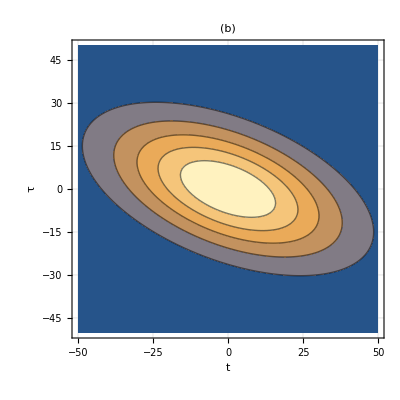

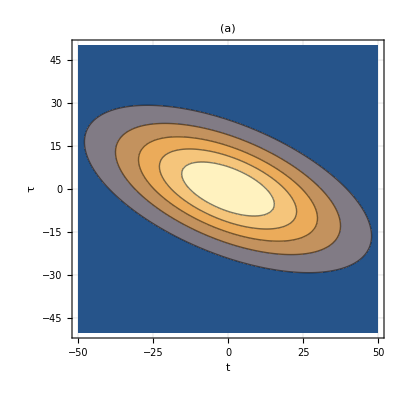

```mathematica
ListContourPlot[classical6,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(b)",PlotRange->Full,Contours-> 5,ImageSize->Scaled[0.5]]
ListContourPlot[quanalytical6,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"(a)",PlotRange->Full,Contours->5,ImageSize->Scaled[0.5]]
```

### Experiment 7: Classical only, Range: 50, Manipulate B_i

```mathematica
Manipulate[
range=50;
σFtest=0.1;
classical7=Table[N[Classical[σFtest,t-range -1,τ-range -1,0,0,0,10,b2,b3]],{t,1,2 range +1},{τ,1,2 range +1}];
classical7=classical7/Total[Total[classical7]];
ListContourPlot[classical7,DataRange->{{-range,range},{-range,range}}, AxesLabel->{"t","τ"},LabelStyle->{FontSize->60,FontFamily->"Times", ,Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotLabel->"Classical (Manipulate)",PlotRange->Full,Contours->5,ImageSize->Scaled[0.5]],{b2,-20,20},{b3,-30,30}]
```

## Backup of results

```mathematica
classical1={{0.00186252418464439,0.0018957613153028198,0.0019276369761878401,0.001958063155055188,0.0019869548457161668,0.002014230442522438,0.0020398121235250784,0.0020636262197963927,0.0020856035684659515,0.002105679847106153,0.002123795887206744,0.002139897964601506,0.0021539380648527844,0.002165874121759628,0.002175670227331641,0.0021832968117618443,0.002188730792136175,0.0021919556888329596,0.0021929617087909025,0.002191745795056759,0.0021883116422618436},{0.0019247241574007507,0.0019574929072127536,0.0019888029358759085,0.002018566972481413,0.002046701129421608,0.00207312529535428,0.0020977635145878575,0.0021205443503778906,0.0021414012297062686,0.0021602727672165724,0.0021771030661010228,0.0021918419938758474,0.002204445431141406,0.002214875491599832,0.002223100711794764,0.0022290962092433382,0.002232843807848179,0.002234332129704762,0.0022335566526551537,0.002230519733180698,0.0022252305944714433},{0.001983817824420852,0.0020159671529466935,0.0020465623049707215,0.0020755172401798272,0.00210274967747607,0.0021281814838001976,0.002151739047111416,0.0021733536310352777,0.0021929617087909025,0.0022105052741287637,0.0022259321271500703,0.0022391961330373213,0.0022502574519015846,0.0022590827381440423,0.0022656453079356793,0.0022699252736378974,0.0022719096442163733,0.0022715923909386103,0.0022689744778902044,0.002264063857093636,0.0022568754282641804},{0.0020393970801360402,0.002070777419163272,0.0021005107250586376,0.0021285126792803294,0.002154703093459502,0.0021790062914278006,0.002201351473149798,0.0022216730581136605,0.0022399110058509155,0.0022560111113940685,0.0022699252736378974,0.002281611734745367,0.002291035288930727,0.0022981674591589386,0.0023029866405202843,0.0023054782092699014,0.002305634596762066,0.002303455327756087,0.0022989470228224804,0.0022921233648323784,0.0022830050297675533},{0.0020910697171809627,0.0021215345253400753,0.0021502628431244106,0.0021771725610516546,0.0022021860621373717,0.0022252305944714433,0.002246238623486543,0.002265148161533458,0.0022819030725135655,0.0022964533494740052,0.0023087553632448114,0.0023187720803880827,0.002326473248935545,0.002331835550610812,0.0023348427184644006,0.002335485619090948,0.002333762298847085,0.0023296779937426273,0.0023232451029350175,0.002314483126014784,0.0023034185645259713},{0.002138464014170742,0.00216787132699095,0.0021954568791712177,0.0022211412477980454,0.0022448498524758136,0.0022665133158330914,0.002286067801571905,0.002303455327756087,0.0023186240531877507,0.0023315285348928455,0.0023421299549262115,0.0023503963149120325,0.0023563025969552498,0.002359830889791483,0.002360970479285232,0.002359717902636425,0.0023560769659114905,0.0023500587247747397,0.0023416814285565904,0.0023309704280546325,0.002317958047719461},{0.002181233175538044,0.002209447126708789,0.0022357589973551833,0.002260092512985444,0.0022823765757312487,0.00230254561023715,0.0023205398850327063,0.0023363058071840448,0.0023497961881912,0.002360970479285232,0.0023697949744832516,0.002376242979978329,0.0023802949486729326,0.002381938578906985,0.002381168876682648,0.0023779881809453504,0.0023724061517419385,0.002364439721339859,0.0023541130086535363,0.002341457197583217,0.002326510380125127},{0.002219059549495182,0.0022459518391111286,0.002270867406937189,0.002293733567340705,0.002314483126014784,0.002333054708812084,0.002349393064114189,0.0023634493366523823,0.002375181310880956,0.002384553622206495,0.002391537934594044,0.0023961130833018633,0.0023982651817385284,0.002397987691687348,0.002395281456401071,0.0023901546963324568,0.0023826229675309478,0.002372709083000129,0.0023604429975723792,0.0023458616571138103,0.0023290088131218824},{0.002251658552502509,0.0022771098385876844,0.0023005161226839653,0.0023218087215033925,0.002340924735071624,0.0023578073562099283,0.0023724061517419385,0.0023846773134773825,0.0023945838772249295,0.002402095908301872,0.002407190652237711,0.0024098526496098356,0.0024100738142001977,0.002407853473920005,0.002403198374212545,0.0023961226439100395,0.0023866477237863854,0.0023748022583114405,0.0023606219513716705,0.0023441493869742086,0.002325433816194419},{0.002278782232499335,0.002302683423127136,0.002324478319228431,0.002344102621181547,0.002361498078872974,0.0023766127797067143,0.0023894014066853917,0.0023998254647677126,0.002407853473920005,0.002413461127506937,0.0024166314149060954,0.002417354707480776,0.0024156288073028764,0.0024114589582808453,0.0024048578196138315,0.002395845401760107,0.002384448965373041,0.0023707028839189846,0.002354648470946015,0.0023363337732183053,0.0023158133311657093},{0.002300222408528899,0.0023224758333634907,0.0023425692202411605,0.0023604429975723792,0.002376043880881635,0.002389325137428757,0.0024002468194264086,0.00240877596422502,0.002414886760061269,0.002418560676203703,0.0024197865565771196,0.002418560676203703,0.002414886760061269,0.00240877596422502,0.0024002468194264086,0.002389325137428757,0.002376043880881635,0.0023604429975723792,0.0023425692202411605,0.0023224758333634907,0.002300222408528899},{0.0023158133311657093,0.0023363337732183053,0.002354648470946015,0.0023707028839189846,0.002384448965373041,0.002395845401760107,0.0024048578196138315,0.0024114589582808453,0.0024156288073028764,0.002417354707480776,0.0024166314149060954,0.002413461127506937,0.002407853473920005,0.0023998254647677126,0.0023894014066853917,0.0023766127797067143,0.002361498078872974,0.002344102621181547,0.002324478319228431,0.002302683423127136,0.002278782232499335},{0.002325433816194419,0.0023441493869742086,0.0023606219513716705,0.0023748022583114405,0.0023866477237863854,0.0023961226439100395,0.002403198374212545,0.002407853473920005,0.0024100738142001977,0.0024098526496098356,0.002407190652237711,0.002402095908301872,0.0023945838772249295,0.0023846773134773825,0.0023724061517419385,0.0023578073562099283,0.002340924735071624,0.0023218087215033925,0.0023005161226839653,0.0022771098385876844,0.002251658552502509},{0.0023290088131218824,0.0023458616571138103,0.0023604429975723792,0.002372709083000129,0.0023826229675309478,0.0023901546963324568,0.002395281456401071,0.002397987691687348,0.0023982651817385284,0.0023961130833018633,0.002391537934594044,0.002384553622206495,0.002375181310880956,0.0023634493366523823,0.002349393064114189,0.002333054708812084,0.002314483126014784,0.002293733567340705,0.002270867406937189,0.0022459518391111286,0.002219059549495182},{0.002326510380125127,0.002341457197583217,0.0023541130086535363,0.002364439721339859,0.0023724061517419385,0.0023779881809453504,0.002381168876682648,0.002381938578906985,0.0023802949486729326,0.002376242979978329,0.0023697949744832516,0.002360970479285232,0.0023497961881912,0.0023363058071840448,0.0023205398850327063,0.00230254561023715,0.0022823765757312487,0.002260092512985444,0.0022357589973551833,0.002209447126708789,0.002181233175538044},{0.002317958047719461,0.0023309704280546325,0.0023416814285565904,0.0023500587247747397,0.0023560769659114905,0.002359717902636425,0.002360970479285232,0.002359830889791483,0.0023563025969552498,0.0023503963149120325,0.0023421299549262115,0.0023315285348928455,0.0023186240531877507,0.002303455327756087,0.002286067801571905,0.0022665133158330914,0.0022448498524758136,0.0022211412477980454,0.0021954568791712177,0.00216787132699095,0.002138464014170742},{0.0023034185645259713,0.002314483126014784,0.0023232451029350175,0.0023296779937426273,0.002333762298847085,0.002335485619090948,0.0023348427184644006,0.002331835550610812,0.002326473248935545,0.0023187720803880827,0.0023087553632448114,0.0022964533494740052,0.0022819030725135655,0.002265148161533458,0.002246238623486543,0.0022252305944714433,0.0022021860621373717,0.0021771725610516546,0.0021502628431244106,0.0021215345253400753,0.0020910697171809627},{0.0022830050297675533,0.0022921233648323784,0.0022989470228224804,0.002303455327756087,0.002305634596762066,0.0023054782092699014,0.0023029866405202843,0.0022981674591589386,0.002291035288930727,0.002281611734745367,0.0022699252736378974,0.0022560111113940685,0.0022399110058509155,0.0022216730581136605,0.002201351473149798,0.0021790062914278006,0.002154703093459502,0.0021285126792803294,0.0021005107250586376,0.002070777419163272,0.0020393970801360402},{0.0022568754282641804,0.002264063857093636,0.0022689744778902044,0.0022715923909386103,0.0022719096442163733,0.0022699252736378974,0.0022656453079356793,0.0022590827381440423,0.0022502574519015846,0.0022391961330373213,0.0022259321271500703,0.0022105052741287637,0.0021929617087909025,0.0021733536310352777,0.002151739047111416,0.0021281814838001976,0.00210274967747607,0.0020755172401798272,0.0020465623049707215,0.0020159671529466935,0.001983817824420852},{0.0022252305944714433,0.002230519733180698,0.0022335566526551537,0.002234332129704762,0.002232843807848179,0.0022290962092433382,0.002223100711794764,0.002214875491599832,0.002204445431141406,0.0021918419938758474,0.0021771030661010228,0.0021602727672165724,0.0021414012297062686,0.0021205443503778906,0.0020977635145878575,0.00207312529535428,0.002046701129421608,0.002018566972481413,0.0019888029358759085,0.0019574929072127536,0.0019247241574007507},{0.0021883116422618436,0.002191745795056759,0.0021929617087909025,0.0021919556888329596,0.002188730792136175,0.0021832968117618443,0.002175670227331641,0.002165874121759628,0.0021539380648527844,0.002139897964601506,0.002123795887206744,0.002105679847106153,0.0020856035684659515,0.0020636262197963927,0.0020398121235250784,0.002014230442522438,0.0019869548457161668,0.001958063155055188,0.0019276369761878401,0.0018957613153028198,0.00186252418464439}};
```

```mathematica
quanalytical1={{1.7351494003708536*^-12,6.132297814455202*^-12,2.0876361950322134*^-11,6.845916754844806*^-11,2.1624876005153667*^-10,6.579923647120066*^-10,1.928560637511688*^-9,5.444913175299137*^-9,1.4807912361611108*^-8,3.8791978297956055*^-8,9.788930316929*^-8,2.3794345421034558*^-7,5.571312293294187*^-7,1.2565693440177978*^-6,2.7299873431230773*^-6,5.713207833841576*^-6,0.000011517139537241569,0.000022364255764382317,0.00004183208277593744,0.00007537194840672104,0.0001308142971924584},{3.7977202056711065*^-11,1.2258088068456986*^-10,3.8112525270552833*^-10,1.141452725888211*^-9,3.2930122776501033*^-9,9.151114438757277*^-9,2.4496263166072467*^-8,6.316418659144206*^-8,1.5688708460242286*^-7,3.753606078231889*^-7,8.650782854682752*^-7,1.9204691895633887*^-6,4.1068088901628955*^-6,8.459542156880899*^-6,0.000016785506117615997,0.00003208242874952321,0.0000590670460578529,0.00010475348551473179,0.0001789521532961787,0.0002944764648539224,0.0004667770223590064},{6.608401271830873*^-10,1.9480925540564354*^-9,5.5318192698008135*^-9,1.5131138111582227*^-8,3.986763045932312*^-8,1.0118461157249328*^-7,2.473738166966259*^-7,5.82556707236181*^-7,1.3215022291228955*^-6,2.8876384060097844*^-6,6.078031336013141*^-6,0.000012323335618376305,0.000024067935230488066,0.00004527876866640788,0.00008205321418346785,0.0001432325764297144,0.0002408425552073403,0.00039009453355650357,0.0006086277067635577,0.0009147002327814925,0.0013241923553427041},{9.142336392007413*^-9,2.4614090083101834*^-8,6.383451902344949*^-8,1.5946765624710146*^-7,3.837380358323807*^-7,8.894925221937176*^-7,1.986071917474447*^-6,4.271622407575344*^-6,8.849850974163436*^-6,0.000017661365371765492,0.00003395140950681591,0.00006286900091413274,0.00011213999303993345,0.00019267692513947484,0.0003188923531351526,0.0005083978668056754,0.0007807438108424956,0.001154937803164567,0.0016457120898391163,0.002258886128614869,0.0029866204436415013},{1.0055538617271219*^-7,2.472551437237544*^-7,5.856397521543638*^-7,1.3361677254065273*^-6,2.9365447445423834*^-6,6.216665272980092*^-6,0.000012677206411725156,0.000024902035923852123,0.00004711849009663809,0.00008588020868000586,0.0001507787133941979,0.00025499530916324177,0.0004154029397465791,0.0006518567336144655,0.0009853260452120933,0.0014346731991034271,0.002012200368684735,0.002718533438041361,0.0035378820540578754,0.0044350368996479775,0.005355454586173522},{8.793076052339132*^-7,1.974668665154825*^-6,4.271622407575344*^-6,8.900956805450583*^-6,0.000017865934897421224,0.00003454299715652776,0.0000643338441608823,0.0001154155179007991,0.0001994500377442749,0.00033200854169280727,0.0005323651374625712,0.0008222713790857061,0.0012233929024897693,0.0017533231028680984,0.0024204893174381253,0.0032187674533168463,0.004123075129307988,0.005087426076680401,0.006046724629995433,0.006922890886975839,0.007634841022475474},{6.113130553494106*^-6,0.000012538064057076974,0.00002477094151807624,0.000047141105162245185,0.00008641760414629284,0.00015259837178572917,0.0002595630053110644,0.0004252858216149851,0.0006712189833521206,0.0010204524512214196,0.001494398874931761,0.0021080723245865377,0.002864505745614985,0.0037493769466948406,0.004727306138714476,0.005741343978173105,0.006716741320186767,0.007569181066563001,0.008216453127703176,0.008591422679709472,0.008653484216825278},{0.00003378888511946367,0.00006329276725574806,0.00011420352843194411,0.0001984952763466587,0.00033232732087302676,0.0005359535263891614,0.0008325943036701414,0.0012459050721821939,0.0017958980902636594,0.0024935819149658105,0.003335114945001624,0.004296780709885544,0.005332376292409656,0.006374462994725673,0.007340263252313129,0.008141883491693256,0.008699280755098477,0.008953380203587186,0.008876380754914379,0.008476762889212848,0.007797751009560328},{0.00014848117779799288,0.0002540183168390052,0.00041860448804263424,0.0006644892244714215,0.0010160550091252532,0.0014965516700578291,0.0021233003274089475,0.0029018593154063383,0.0038202034873768323,0.004844420752505792,0.00591755674526751,0.0069628689718862005,0.007891857417157271,0.00861619370345738,0.009061433210893546,0.009179595612337823,0.008957677482220136,0.008420008113682377,0.007623858275357324,0.006649398097378697,0.005586439134616506},{0.000518747833044542,0.0008105192502468615,0.0012198757235957482,0.0017685325577116607,0.00246976565070527,0.0033223367424832875,0.004305035809577171,0.00537347340222622,0.006460686309103599,0.0074825120067416396,0.008347595687555947,0.008970581697251411,0.009285921792709444,0.009259225342146113,0.008893434315005095,0.008228289552732401,0.007333222232946978,0.006295429183815894,0.0052059627421817585,0.004146884929332626,0.0031819117424401553},{0.0014408824026045349,0.0020561224933825025,0.0028262764975715525,0.003742187347851643,0.0047728921530020875,0.005863851083505158,0.00693952045114141,0.0079108145481372,0.008686766807478378,0.009188409433660394,0.00936198047327796,0.009188409433660394,0.008686766807478378,0.0079108145481372,0.00693952045114141,0.005863851083505158,0.0047728921530020875,0.003742187347851643,0.0028262764975715525,0.0020561224933825025,0.0014408824026045349},{0.0031819117424401553,0.004146884929332626,0.0052059627421817585,0.006295429183815894,0.007333222232946978,0.008228289552732401,0.008893434315005095,0.009259225342146113,0.009285921792709444,0.008970581697251411,0.008347595687555947,0.0074825120067416396,0.006460686309103599,0.00537347340222622,0.004305035809577171,0.0033223367424832875,0.00246976565070527,0.0017685325577116607,0.0012198757235957482,0.0008105192502468615,0.000518747833044542},{0.005586439134616506,0.006649398097378697,0.007623858275357324,0.008420008113682377,0.008957677482220136,0.009179595612337823,0.009061433210893546,0.00861619370345738,0.007891857417157271,0.0069628689718862005,0.00591755674526751,0.004844420752505792,0.0038202034873768323,0.0029018593154063383,0.0021233003274089475,0.0014965516700578291,0.0010160550091252532,0.0006644892244714215,0.00041860448804263424,0.0002540183168390052,0.00014848117779799288},{0.007797751009560328,0.008476762889212848,0.008876380754914379,0.008953380203587186,0.008699280755098477,0.008141883491693256,0.007340263252313129,0.006374462994725673,0.005332376292409656,0.004296780709885544,0.003335114945001624,0.0024935819149658105,0.0017958980902636594,0.0012459050721821939,0.0008325943036701414,0.0005359535263891614,0.00033232732087302676,0.0001984952763466587,0.00011420352843194411,0.00006329276725574806,0.00003378888511946367},{0.008653484216825278,0.008591422679709472,0.008216453127703176,0.007569181066563001,0.006716741320186767,0.005741343978173105,0.004727306138714476,0.0037493769466948406,0.002864505745614985,0.0021080723245865377,0.001494398874931761,0.0010204524512214196,0.0006712189833521206,0.0004252858216149851,0.0002595630053110644,0.00015259837178572917,0.00008641760414629284,0.000047141105162245185,0.00002477094151807624,0.000012538064057076974,6.113130553494106*^-6},{0.007634841022475474,0.006922890886975839,0.006046724629995433,0.005087426076680401,0.004123075129307988,0.0032187674533168463,0.0024204893174381253,0.0017533231028680984,0.0012233929024897693,0.0008222713790857061,0.0005323651374625712,0.00033200854169280727,0.0001994500377442749,0.0001154155179007991,0.0000643338441608823,0.00003454299715652776,0.000017865934897421224,8.900956805450583*^-6,4.271622407575344*^-6,1.974668665154825*^-6,8.793076052339132*^-7},{0.005355454586173522,0.0044350368996479775,0.0035378820540578754,0.002718533438041361,0.002012200368684735,0.0014346731991034271,0.0009853260452120933,0.0006518567336144655,0.0004154029397465791,0.00025499530916324177,0.0001507787133941979,0.00008588020868000586,0.00004711849009663809,0.000024902035923852123,0.000012677206411725156,6.216665272980092*^-6,2.9365447445423834*^-6,1.3361677254065273*^-6,5.856397521543638*^-7,2.472551437237544*^-7,1.0055538617271219*^-7},{0.0029866204436415013,0.002258886128614869,0.0016457120898391163,0.001154937803164567,0.0007807438108424956,0.0005083978668056754,0.0003188923531351526,0.00019267692513947484,0.00011213999303993345,0.00006286900091413274,0.00003395140950681591,0.000017661365371765492,8.849850974163436*^-6,4.271622407575344*^-6,1.986071917474447*^-6,8.894925221937176*^-7,3.837380358323807*^-7,1.5946765624710146*^-7,6.383451902344949*^-8,2.4614090083101834*^-8,9.142336392007413*^-9},{0.0013241923553427041,0.0009147002327814925,0.0006086277067635577,0.00039009453355650357,0.0002408425552073403,0.0001432325764297144,0.00008205321418346785,0.00004527876866640788,0.000024067935230488066,0.000012323335618376305,6.078031336013141*^-6,2.8876384060097844*^-6,1.3215022291228955*^-6,5.82556707236181*^-7,2.473738166966259*^-7,1.0118461157249328*^-7,3.986763045932312*^-8,1.5131138111582227*^-8,5.5318192698008135*^-9,1.9480925540564354*^-9,6.608401271830873*^-10},{0.0004667770223590064,0.0002944764648539224,0.0001789521532961787,0.00010475348551473179,0.0000590670460578529,0.00003208242874952321,0.000016785506117615997,8.459542156880899*^-6,4.1068088901628955*^-6,1.9204691895633887*^-6,8.650782854682752*^-7,3.753606078231889*^-7,1.5688708460242286*^-7,6.316418659144206*^-8,2.4496263166072467*^-8,9.151114438757277*^-9,3.2930122776501033*^-9,1.141452725888211*^-9,3.8112525270552833*^-10,1.2258088068456986*^-10,3.7977202056711065*^-11},{0.0001308142971924584,0.00007537194840672104,0.00004183208277593744,0.000022364255764382317,0.000011517139537241569,5.713207833841576*^-6,2.7299873431230773*^-6,1.2565693440177978*^-6,5.571312293294187*^-7,2.3794345421034558*^-7,9.788930316929*^-8,3.8791978297956055*^-8,1.4807912361611108*^-8,5.444913175299137*^-9,1.928560637511688*^-9,6.579923647120066*^-10,2.1624876005153667*^-10,6.845916754844806*^-11,2.0876361950322134*^-11,6.132297814455202*^-12,1.7351494003708536*^-12}};
```

```mathematica
qunumerical1={{9.905293036369354*^-6,0.00001184364509569808,0.000018080157940603758,0.0000283641270864458,0.000041851827321782665,0.00005706086729545819,0.00007178012377418004,0.00008313647666845685,0.00008803154650392668,0.00008400826810387741,0.00007035651755762694,0.00003958882891260646,0.000046651035926047874,0.00005628345022494298,0.00006509902836697012,0.0000712778708712439,0.00007723645819051644,0.00009059539197784856,0.0001227220961079029,0.00018565448135885972,0.00028915373448903323},{0.000019742017775996866,0.00003155897412448114,0.00004587895386090222,0.000060824857407768854,0.00007418543775688412,0.00008348855298441149,0.00008623296547668536,0.00008048059925405995,0.00006580886678617474,0.00004434776638676984,0.00002145385139890704,0.00003852371916870535,0.0000550058329249181,0.0000745400594509352,0.00009906246287084812,0.00013484128945852642,0.00019246523902717843,0.0002847016191937505,0.00042311644355010297,0.00061518790227565,0.0008632173939080408},{0.00005069975737757949,0.00006567499731545386,0.00007761519824797366,0.00008429611636937881,0.00008394691729425404,0.00007553220184960495,0.000059351819461917575,0.00003791802085327743,0.00001676691060474223,4.708403350095681*^-6,0.00001315831011880491,0.00012846180409741532,0.00017417685496139842,0.00023467795547792882,0.0003196254752083039,0.0004418477405089509,0.0006143905711193194,0.0008467861801597832,0.001142285277457601,0.0014973248774507672,0.0019030662762086292},{0.00008166415148999586,0.0000857320838718233,0.00008179856922966309,0.00006990278602323185,0.00005153807690269537,0.00003009113883978056,0.000011487777812923358,4.655991239796306*^-6,0.000021279688795538006,0.0000745209925837193,0.0001768657680716588,0.00039141339294316907,0.0005059542428494481,0.0006578855533625264,0.000860874366007366,0.0011266885840456064,0.0014611627289925749,0.0018616434159797327,0.002317141742500424,0.0028109174079963693,0.003323818076755126},{0.00007974196653148514,0.0000642704540911101,0.00004341327518611836,0.00002193664093874564,6.650285630000812*^-6,6.714081708513341*^-6,0.00003370285245933394,0.00010088165705440809,0.0002214083943254152,0.00040573701067580587,0.0006590193916031874,0.0009211436381566872,0.001152660870965916,0.001444780304463647,0.0018062252356185245,0.002237622780634015,0.0027292970985138324,0.00326220676132179,0.003811636566953993,0.0043517566724426675,0.004858834534817216},{0.000035530806438052025,0.000014562938719616688,3.597247816888997*^-6,0.000012467326856620257,0.00005258741798412816,0.0001366713295127928,0.00027765077376502417,0.00048653783939744564,0.0007696113338630755,0.001125875006339262,0.0015458537127302117,0.0017814643788840738,0.002160591609598226,0.0026076950689954323,0.0031171480693228393,0.0036719092702920783,0.004245304128938858,0.0048057955207705715,0.005322674958884987,0.005770192709538615,0.006128718666850225},{3.122746068350441*^-6,0.000022869076971569473,0.00007921164782132322,0.00018406125900812317,0.0003491355678197048,0.0005847419467941118,0.0008975453721832819,0.00128778429372563,0.001747012462648686,0.0022575419069807284,0.0027941328341924113,0.0029520986901895065,0.0034626088886557404,0.004019182795189775,0.004598054301555173,0.005166389103166169,0.0056879970886621395,0.006129968709177237,0.0064675059109285905,0.006685315471557251,0.0067758893802517955},{0.00011356483713298126,0.00024296479841251506,0.00043660947973330665,0.0007027694505114799,0.0010468431327806354,0.0014693111513475274,0.0019631929189968954,0.0025122232146985784,0.003091001996944884,0.0036676791440266956,0.004208551644270685,0.004291078124876237,0.0048552026456222044,0.005413246609470442,0.0059287067074995925,0.006363688348183867,0.006686153572411738,0.006875209851495233,0.006922534025346231,0.006830106720326371,0.006606277622909388},{0.0005379663466833265,0.0008388256440444399,0.0012173213710253638,0.0016721120414448893,0.002196438426239181,0.0027759914006997627,0.003387508052534216,0.003999544414691973,0.0045759743379407405,0.005081471429264081,0.005487130998395898,0.0055436888764322356,0.006035744649844978,0.006454498185908965,0.006763801720446427,0.006935618737866706,0.0069554014844715115,0.006823413931282565,0.006551918199718499,0.0061601905147118646,0.005670066911050578},{0.0014040868483868752,0.0018927790567164462,0.0024454417801365296,0.003048111521191689,0.0036802722965549334,0.0043137911230616095,0.004913987016659882,0.005443591599676185,0.00586877190980251,0.006165136851499499,0.00632146034124423,0.006409119645521825,0.006696907699473983,0.006854864129109267,0.006861801909958429,0.006711246710262771,0.0064124520343362785,0.00598718660484037,0.005463979868785872,0.0048726049019397035,0.0042408608644882596},{0.0027032332807621533,0.003324665873866264,0.00396695440665401,0.0046056577122016865,0.005210954102521637,0.005748625684242479,0.006183919565965391,0.00648762615827887,0.006642152662468692,0.006645045245086637,0.00650844529166432,0.006645045245086637,0.006642152662468692,0.00648762615827887,0.006183919565965391,0.005748625684242479,0.005210954102521637,0.0046056577122016865,0.00396695440665401,0.003324665873866264,0.0027032332807621533},{0.0042408608644882596,0.0048726049019397035,0.005463979868785872,0.00598718660484037,0.0064124520343362785,0.006711246710262771,0.006861801909958429,0.006854864129109267,0.006696907699473983,0.006409119645521825,0.00632146034124423,0.006165136851499499,0.00586877190980251,0.005443591599676185,0.004913987016659882,0.0043137911230616095,0.0036802722965549334,0.003048111521191689,0.0024454417801365296,0.0018927790567164462,0.0014040868483868752},{0.005670066911050578,0.0061601905147118646,0.006551918199718499,0.006823413931282565,0.0069554014844715115,0.006935618737866706,0.006763801720446427,0.006454498185908965,0.006035744649844978,0.0055436888764322356,0.005487130998395898,0.005081471429264081,0.0045759743379407405,0.003999544414691973,0.003387508052534216,0.0027759914006997627,0.002196438426239181,0.0016721120414448893,0.0012173213710253638,0.0008388256440444399,0.0005379663466833265},{0.006606277622909388,0.006830106720326371,0.006922534025346231,0.006875209851495233,0.006686153572411738,0.006363688348183867,0.0059287067074995925,0.005413246609470442,0.0048552026456222044,0.004291078124876237,0.004208551644270685,0.0036676791440266956,0.003091001996944884,0.0025122232146985784,0.0019631929189968954,0.0014693111513475274,0.0010468431327806354,0.0007027694505114799,0.00043660947973330665,0.00024296479841251506,0.00011356483713298126},{0.0067758893802517955,0.006685315471557251,0.0064675059109285905,0.006129968709177237,0.0056879970886621395,0.005166389103166169,0.004598054301555173,0.004019182795189775,0.0034626088886557404,0.0029520986901895065,0.0027941328341924113,0.0022575419069807284,0.001747012462648686,0.00128778429372563,0.0008975453721832819,0.0005847419467941118,0.0003491355678197048,0.00018406125900812317,0.00007921164782132322,0.000022869076971569473,3.122746068350441*^-6},{0.006128718666850225,0.005770192709538615,0.005322674958884987,0.0048057955207705715,0.004245304128938858,0.0036719092702920783,0.0031171480693228393,0.0026076950689954323,0.002160591609598226,0.0017814643788840738,0.0015458537127302117,0.001125875006339262,0.0007696113338630755,0.00048653783939744564,0.00027765077376502417,0.0001366713295127928,0.00005258741798412816,0.000012467326856620257,3.597247816888997*^-6,0.000014562938719616688,0.000035530806438052025},{0.004858834534817216,0.0043517566724426675,0.003811636566953993,0.00326220676132179,0.0027292970985138324,0.002237622780634015,0.0018062252356185245,0.001444780304463647,0.001152660870965916,0.0009211436381566872,0.0006590193916031874,0.00040573701067580587,0.0002214083943254152,0.00010088165705440809,0.00003370285245933394,6.714081708513341*^-6,6.650285630000812*^-6,0.00002193664093874564,0.00004341327518611836,0.0000642704540911101,0.00007974196653148514},{0.003323818076755126,0.0028109174079963693,0.002317141742500424,0.0018616434159797327,0.0014611627289925749,0.0011266885840456064,0.000860874366007366,0.0006578855533625264,0.0005059542428494481,0.00039141339294316907,0.0001768657680716588,0.0000745209925837193,0.000021279688795538006,4.655991239796306*^-6,0.000011487777812923358,0.00003009113883978056,0.00005153807690269537,0.00006990278602323185,0.00008179856922966309,0.0000857320838718233,0.00008166415148999586},{0.0019030662762086292,0.0014973248774507672,0.001142285277457601,0.0008467861801597832,0.0006143905711193194,0.0004418477405089509,0.0003196254752083039,0.00023467795547792882,0.00017417685496139842,0.00012846180409741532,0.00001315831011880491,4.708403350095681*^-6,0.00001676691060474223,0.00003791802085327743,0.000059351819461917575,0.00007553220184960495,0.00008394691729425404,0.00008429611636937881,0.00007761519824797366,0.00006567499731545386,0.00005069975737757949},{0.0008632173939080408,0.00061518790227565,0.00042311644355010297,0.0002847016191937505,0.00019246523902717843,0.00013484128945852642,0.00009906246287084812,0.0000745400594509352,0.0000550058329249181,0.00003852371916870535,0.00002145385139890704,0.00004434776638676984,0.00006580886678617474,0.00008048059925405995,0.00008623296547668536,0.00008348855298441149,0.00007418543775688412,0.000060824857407768854,0.00004587895386090222,0.00003155897412448114,0.000019742017775996866},{0.00028915373448903323,0.00018565448135885972,0.0001227220961079029,0.00009059539197784856,0.00007723645819051644,0.0000712778708712439,0.00006509902836697012,0.00005628345022494298,0.000046651035926047874,0.00003958882891260646,0.00007035651755762694,0.00008400826810387741,0.00008803154650392668,0.00008313647666845685,0.00007178012377418004,0.00005706086729545819,0.000041851827321782665,0.0000283641270864458,0.000018080157940603758,0.00001184364509569808,9.905293036369354*^-6}};
```

```mathematica
classical2={{0.00186252418464439,0.0018957613153028198,0.0019276369761878401,0.001958063155055188,0.0019869548457161668,0.002014230442522438,0.0020398121235250784,0.0020636262197963927,0.0020856035684659515,0.002105679847106153,0.002123795887206744,0.002139897964601506,0.0021539380648527844,0.002165874121759628,0.002175670227331641,0.0021832968117618443,0.002188730792136175,0.0021919556888329596,0.0021929617087909025,0.002191745795056759,0.0021883116422618436},{0.0019247241574007507,0.0019574929072127536,0.0019888029358759085,0.002018566972481413,0.002046701129421608,0.00207312529535428,0.0020977635145878575,0.0021205443503778906,0.0021414012297062686,0.0021602727672165724,0.0021771030661010228,0.0021918419938758474,0.002204445431141406,0.002214875491599832,0.002223100711794764,0.0022290962092433382,0.002232843807848179,0.002234332129704762,0.0022335566526551537,0.002230519733180698,0.0022252305944714433},{0.001983817824420852,0.0020159671529466935,0.0020465623049707215,0.0020755172401798272,0.00210274967747607,0.0021281814838001976,0.002151739047111416,0.0021733536310352777,0.0021929617087909025,0.0022105052741287637,0.0022259321271500703,0.0022391961330373213,0.0022502574519015846,0.0022590827381440423,0.0022656453079356793,0.0022699252736378974,0.0022719096442163733,0.0022715923909386103,0.0022689744778902044,0.002264063857093636,0.0022568754282641804},{0.0020393970801360402,0.002070777419163272,0.0021005107250586376,0.0021285126792803294,0.002154703093459502,0.0021790062914278006,0.002201351473149798,0.0022216730581136605,0.0022399110058509155,0.0022560111113940685,0.0022699252736378974,0.002281611734745367,0.002291035288930727,0.0022981674591589386,0.0023029866405202843,0.0023054782092699014,0.002305634596762066,0.002303455327756087,0.0022989470228224804,0.0022921233648323784,0.0022830050297675533},{0.0020910697171809627,0.0021215345253400753,0.0021502628431244106,0.0021771725610516546,0.0022021860621373717,0.0022252305944714433,0.002246238623486543,0.002265148161533458,0.0022819030725135655,0.0022964533494740052,0.0023087553632448114,0.0023187720803880827,0.002326473248935545,0.002331835550610812,0.0023348427184644006,0.002335485619090948,0.002333762298847085,0.0023296779937426273,0.0023232451029350175,0.002314483126014784,0.0023034185645259713},{0.002138464014170742,0.00216787132699095,0.0021954568791712177,0.0022211412477980454,0.0022448498524758136,0.0022665133158330914,0.002286067801571905,0.002303455327756087,0.0023186240531877507,0.0023315285348928455,0.0023421299549262115,0.0023503963149120325,0.0023563025969552498,0.002359830889791483,0.002360970479285232,0.002359717902636425,0.0023560769659114905,0.0023500587247747397,0.0023416814285565904,0.0023309704280546325,0.002317958047719461},{0.002181233175538044,0.002209447126708789,0.0022357589973551833,0.002260092512985444,0.0022823765757312487,0.00230254561023715,0.0023205398850327063,0.0023363058071840448,0.0023497961881912,0.002360970479285232,0.0023697949744832516,0.002376242979978329,0.0023802949486729326,0.002381938578906985,0.002381168876682648,0.0023779881809453504,0.0023724061517419385,0.002364439721339859,0.0023541130086535363,0.002341457197583217,0.002326510380125127},{0.002219059549495182,0.0022459518391111286,0.002270867406937189,0.002293733567340705,0.002314483126014784,0.002333054708812084,0.002349393064114189,0.0023634493366523823,0.002375181310880956,0.002384553622206495,0.002391537934594044,0.0023961130833018633,0.0023982651817385284,0.002397987691687348,0.002395281456401071,0.0023901546963324568,0.0023826229675309478,0.002372709083000129,0.0023604429975723792,0.0023458616571138103,0.0023290088131218824},{0.002251658552502509,0.0022771098385876844,0.0023005161226839653,0.0023218087215033925,0.002340924735071624,0.0023578073562099283,0.0023724061517419385,0.0023846773134773825,0.0023945838772249295,0.002402095908301872,0.002407190652237711,0.0024098526496098356,0.0024100738142001977,0.002407853473920005,0.002403198374212545,0.0023961226439100395,0.0023866477237863854,0.0023748022583114405,0.0023606219513716705,0.0023441493869742086,0.002325433816194419},{0.002278782232499335,0.002302683423127136,0.002324478319228431,0.002344102621181547,0.002361498078872974,0.0023766127797067143,0.0023894014066853917,0.0023998254647677126,0.002407853473920005,0.002413461127506937,0.0024166314149060954,0.002417354707480776,0.0024156288073028764,0.0024114589582808453,0.0024048578196138315,0.002395845401760107,0.002384448965373041,0.0023707028839189846,0.002354648470946015,0.0023363337732183053,0.0023158133311657093},{0.002300222408528899,0.0023224758333634907,0.0023425692202411605,0.0023604429975723792,0.002376043880881635,0.002389325137428757,0.0024002468194264086,0.00240877596422502,0.002414886760061269,0.002418560676203703,0.0024197865565771196,0.002418560676203703,0.002414886760061269,0.00240877596422502,0.0024002468194264086,0.002389325137428757,0.002376043880881635,0.0023604429975723792,0.0023425692202411605,0.0023224758333634907,0.002300222408528899},{0.0023158133311657093,0.0023363337732183053,0.002354648470946015,0.0023707028839189846,0.002384448965373041,0.002395845401760107,0.0024048578196138315,0.0024114589582808453,0.0024156288073028764,0.002417354707480776,0.0024166314149060954,0.002413461127506937,0.002407853473920005,0.0023998254647677126,0.0023894014066853917,0.0023766127797067143,0.002361498078872974,0.002344102621181547,0.002324478319228431,0.002302683423127136,0.002278782232499335},{0.002325433816194419,0.0023441493869742086,0.0023606219513716705,0.0023748022583114405,0.0023866477237863854,0.0023961226439100395,0.002403198374212545,0.002407853473920005,0.0024100738142001977,0.0024098526496098356,0.002407190652237711,0.002402095908301872,0.0023945838772249295,0.0023846773134773825,0.0023724061517419385,0.0023578073562099283,0.002340924735071624,0.0023218087215033925,0.0023005161226839653,0.0022771098385876844,0.002251658552502509},{0.0023290088131218824,0.0023458616571138103,0.0023604429975723792,0.002372709083000129,0.0023826229675309478,0.0023901546963324568,0.002395281456401071,0.002397987691687348,0.0023982651817385284,0.0023961130833018633,0.002391537934594044,0.002384553622206495,0.002375181310880956,0.0023634493366523823,0.002349393064114189,0.002333054708812084,0.002314483126014784,0.002293733567340705,0.002270867406937189,0.0022459518391111286,0.002219059549495182},{0.002326510380125127,0.002341457197583217,0.0023541130086535363,0.002364439721339859,0.0023724061517419385,0.0023779881809453504,0.002381168876682648,0.002381938578906985,0.0023802949486729326,0.002376242979978329,0.0023697949744832516,0.002360970479285232,0.0023497961881912,0.0023363058071840448,0.0023205398850327063,0.00230254561023715,0.0022823765757312487,0.002260092512985444,0.0022357589973551833,0.002209447126708789,0.002181233175538044},{0.002317958047719461,0.0023309704280546325,0.0023416814285565904,0.0023500587247747397,0.0023560769659114905,0.002359717902636425,0.002360970479285232,0.002359830889791483,0.0023563025969552498,0.0023503963149120325,0.0023421299549262115,0.0023315285348928455,0.0023186240531877507,0.002303455327756087,0.002286067801571905,0.0022665133158330914,0.0022448498524758136,0.0022211412477980454,0.0021954568791712177,0.00216787132699095,0.002138464014170742},{0.0023034185645259713,0.002314483126014784,0.0023232451029350175,0.0023296779937426273,0.002333762298847085,0.002335485619090948,0.0023348427184644006,0.002331835550610812,0.002326473248935545,0.0023187720803880827,0.0023087553632448114,0.0022964533494740052,0.0022819030725135655,0.002265148161533458,0.002246238623486543,0.0022252305944714433,0.0022021860621373717,0.0021771725610516546,0.0021502628431244106,0.0021215345253400753,0.0020910697171809627},{0.0022830050297675533,0.0022921233648323784,0.0022989470228224804,0.002303455327756087,0.002305634596762066,0.0023054782092699014,0.0023029866405202843,0.0022981674591589386,0.002291035288930727,0.002281611734745367,0.0022699252736378974,0.0022560111113940685,0.0022399110058509155,0.0022216730581136605,0.002201351473149798,0.0021790062914278006,0.002154703093459502,0.0021285126792803294,0.0021005107250586376,0.002070777419163272,0.0020393970801360402},{0.0022568754282641804,0.002264063857093636,0.0022689744778902044,0.0022715923909386103,0.0022719096442163733,0.0022699252736378974,0.0022656453079356793,0.0022590827381440423,0.0022502574519015846,0.0022391961330373213,0.0022259321271500703,0.0022105052741287637,0.0021929617087909025,0.0021733536310352777,0.002151739047111416,0.0021281814838001976,0.00210274967747607,0.0020755172401798272,0.0020465623049707215,0.0020159671529466935,0.001983817824420852},{0.0022252305944714433,0.002230519733180698,0.0022335566526551537,0.002234332129704762,0.002232843807848179,0.0022290962092433382,0.002223100711794764,0.002214875491599832,0.002204445431141406,0.0021918419938758474,0.0021771030661010228,0.0021602727672165724,0.0021414012297062686,0.0021205443503778906,0.0020977635145878575,0.00207312529535428,0.002046701129421608,0.002018566972481413,0.0019888029358759085,0.0019574929072127536,0.0019247241574007507},{0.0021883116422618436,0.002191745795056759,0.0021929617087909025,0.0021919556888329596,0.002188730792136175,0.0021832968117618443,0.002175670227331641,0.002165874121759628,0.0021539380648527844,0.002139897964601506,0.002123795887206744,0.002105679847106153,0.0020856035684659515,0.0020636262197963927,0.0020398121235250784,0.002014230442522438,0.0019869548457161668,0.001958063155055188,0.0019276369761878401,0.0018957613153028198,0.00186252418464439}};
```

```mathematica
quanalytical2={{0.0013927274449839135,0.0014538251615042349,0.0015141253537175802,0.0015733128363936083,0.0016310675364918932,0.0016870672914577798,0.0017409907778367863,0.0017925205340385065,0.0018413460382636763,0.0018871668004196032,0.001929695425356087,0.00196866060400887,0.002003809989077235,0.002034912912706322,0.002061762905294394,0.002084179976983679,0.0021020126265847206,0.0021151395465749076,0.0021234709973312377,0.0021269498288195923,0.0021255521334683147},{0.0015082235533794407,0.0015710634955932192,0.00163277130867717,0.0016930141444163767,0.001751456745283994,0.0018077644833136414,0.0018616065000415496,0.0019126589071478304,0.001960608005094243,0.0020051534754426652,0.0020460115017001,0.0020829177735120635,0.0021156303298384273,0.0021439321983972876,0.002167633791136908,0.0021865750187576053,0.002200627091300233,0.002209693976473489,0.0022137134926203395,0.0022126580189220056,0.0022065348114920034},{0.0016232656081917075,0.0016873282521355122,0.0017498997645711166,0.0018106327471704307,0.0018691802020728056,0.0019251987795616738,0.0019783520920414513,0.0020283140502189447,0.002074772175660623,0.002117430842963275,0.002156014404683272,0.0021902701529429407,0.0022199710732762174,0.0022449183487744445,0.002264943575911534,0.0022799106575109103,0.002289717343091207,0.0022942963922034116,0.002293616342243888,0.002287681868478012,0.002276533730511247},{0.001736351873540601,0.0018010663105258345,0.001863911419062233,0.001924528907896689,0.001982563984353478,0.0020376687709471567,0.0020895057485675835,0.0021377511790485505,0.002182098458900993,0.002222261355827002,0.002257977080358296,0.0022890091465888607,0.0023151499784820474,0.002336223221592561,0.0023520857241984905,0.002362629156713402,0.002367781243751788,0.0023675065892453874,0.0023618070814327864,0.002350721871240008,0.002334326924398364},{0.0018459085286969207,0.0019106630764833628,0.0019731570299381437,0.0020330253358034032,0.0020899097702253133,0.002143462477132643,0.0021933494892907054,0.002239254182524342,0.0022808806133630816,0.0023179566910365617,0.002350237136347151,0.0023775061824565006,0.0023995799760093126,0.002416308641225981,0.0024275779745509597,0.002433310743052831,0.002433467565925694,0.002428047365017207,0.0024170873771729184,0.0024006627281991846,0.0023788855752636313},{0.0019503245908477347,0.0020144792719515286,0.0020759759268166285,0.0021344472522752825,0.0021895362711763303,0.002240899939210336,0.0022882126873429542,0.0023311698489290197,0.00236949092119636,0.002402922612350487,0.002431241628047606,0.002454257154380539,0.0024718129987655463,0.0024837893551325333,0.0024901041655129106,0.0024907140563779273,0.0024856148347809403,0.002474841536364286,0.0024584680244618337,0.002436606146714521,0.002409404462670457},{0.0020479903253823005,0.0021108908579214156,0.0021707372603094674,0.002227164760897304,0.0022798225001622865,0.002328377147993094,0.002372516407519845,0.0024119523541311612,0.002446424559836197,0.002475702955599786,0.002499590387670573,0.0025179248281812744,0.002530581205352135,0.0025374728243789703,0.0025385523564245022,0.0025338123799300886,0.002523285465586892,0.00250704380360553,0.0024851983792512486,0.002457897709816932,0.002425326163141153},{0.002137337908682778,0.002198330770187534,0.002255882590044931,0.002309636051575963,0.002359251342692278,0.002404409722738737,0.002444816926130783,0.002480206352047796,0.002510341991875177,0.0025350210494581664,0.002554076213486185,0.0025673775463934297,0.002574833959945311,0.002576394254069451,0.0025720477023574062,0.002561824174870528,0.0025457937962830527,0.002524066144835733,0.002496789004900905,0.0024641466930247005,0.002426357983970453},{0.002216882935544378,0.002275330992515649,0.0023299682769495835,0.0023804498546136474,0.0024264518076285075,0.0024676746890034194,0.002503846764918613,0.0025347269957076805,0.002560107709825972,0.0025798169293239203,0.002593720310403533,0.0026017226684283113,0.002603769063169944,0.0025998454269822884,0.002589978725854941,0.0025742366507670194,0.0025527268442831555,0.0025255956747533867,0.0024930265776445327,0.002455237990296837,0.0024124809126303804},{0.0022852652514633687,0.002340563401787138,0.0023917060790450187,0.0024383655197906177,0.002480238320267224,0.0025170487178726316,0.0025485516134400336,0.0025745352880337065,0.0025948237721491432,0.0026092788302364395,0.002617801529240335,0.0026203333662593634,0.002616856937343337,0.0026073961367334814,0.002592015883354411,0.0025708213789376196,0.0025439569096366004,0.002511604210230495,0.00247398041685905,0.0024313356405489205,0.002383950199455631},{0.002341287548659655,0.002392877803781515,0.00244000036084223,0.0024823491340447584,0.002519645487185266,0.0025516412844659945,0.0025781216386873444,0.002598907314258178,0.00261385674744017,0.0026228676519738404,0.002625878184610911,0.0026228676519738404,0.00261385674744017,0.002598907314258178,0.0025781216386873444,0.0025516412844659945,0.002519645487185266,0.0024823491340447584,0.00244000036084223,0.002392877803781515,0.002341287548659655},{0.002383950199455631,0.0024313356405489205,0.00247398041685905,0.002511604210230495,0.0025439569096366004,0.0025708213789376196,0.002592015883354411,0.0026073961367334814,0.002616856937343337,0.0026203333662593634,0.002617801529240335,0.0026092788302364395,0.0025948237721491432,0.0025745352880337065,0.0025485516134400336,0.0025170487178726316,0.002480238320267224,0.0024383655197906177,0.0023917060790450187,0.002340563401787138,0.0022852652514633687},{0.0024124809126303804,0.002455237990296837,0.0024930265776445327,0.0025255956747533867,0.0025527268442831555,0.0025742366507670194,0.002589978725854941,0.0025998454269822884,0.002603769063169944,0.0026017226684283113,0.002593720310403533,0.0025798169293239203,0.002560107709825972,0.0025347269957076805,0.002503846764918613,0.0024676746890034194,0.0024264518076285075,0.0023804498546136474,0.0023299682769495835,0.002275330992515649,0.002216882935544378},{0.002426357983970453,0.0024641466930247005,0.002496789004900905,0.002524066144835733,0.0025457937962830527,0.002561824174870528,0.0025720477023574062,0.002576394254069451,0.002574833959945311,0.0025673775463934297,0.002554076213486185,0.0025350210494581664,0.002510341991875177,0.002480206352047796,0.002444816926130783,0.002404409722738737,0.002359251342692278,0.002309636051575963,0.002255882590044931,0.002198330770187534,0.002137337908682778},{0.002425326163141153,0.002457897709816932,0.0024851983792512486,0.00250704380360553,0.002523285465586892,0.0025338123799300886,0.0025385523564245022,0.0025374728243789703,0.002530581205352135,0.0025179248281812744,0.002499590387670573,0.002475702955599786,0.002446424559836197,0.0024119523541311612,0.002372516407519845,0.002328377147993094,0.0022798225001622865,0.002227164760897304,0.0021707372603094674,0.0021108908579214156,0.0020479903253823005},{0.002409404462670457,0.002436606146714521,0.0024584680244618337,0.002474841536364286,0.0024856148347809403,0.0024907140563779273,0.0024901041655129106,0.0024837893551325333,0.0024718129987655463,0.002454257154380539,0.002431241628047606,0.002402922612350487,0.00236949092119636,0.0023311698489290197,0.0022882126873429542,0.002240899939210336,0.0021895362711763303,0.0021344472522752825,0.0020759759268166285,0.0020144792719515286,0.0019503245908477347},{0.0023788855752636313,0.0024006627281991846,0.0024170873771729184,0.002428047365017207,0.002433467565925694,0.002433310743052831,0.0024275779745509597,0.002416308641225981,0.0023995799760093126,0.0023775061824565006,0.002350237136347151,0.0023179566910365617,0.0022808806133630816,0.002239254182524342,0.0021933494892907054,0.002143462477132643,0.0020899097702253133,0.0020330253358034032,0.0019731570299381437,0.0019106630764833628,0.0018459085286969207},{0.002334326924398364,0.002350721871240008,0.0023618070814327864,0.0023675065892453874,0.002367781243751788,0.002362629156713402,0.0023520857241984905,0.002336223221592561,0.0023151499784820474,0.0022890091465888607,0.002257977080358296,0.002222261355827002,0.002182098458900993,0.0021377511790485505,0.0020895057485675835,0.0020376687709471567,0.001982563984353478,0.001924528907896689,0.001863911419062233,0.0018010663105258345,0.001736351873540601},{0.002276533730511247,0.002287681868478012,0.002293616342243888,0.0022942963922034116,0.002289717343091207,0.0022799106575109103,0.002264943575911534,0.0022449183487744445,0.0022199710732762174,0.0021902701529429407,0.002156014404683272,0.002117430842963275,0.002074772175660623,0.0020283140502189447,0.0019783520920414513,0.0019251987795616738,0.0018691802020728056,0.0018106327471704307,0.0017498997645711166,0.0016873282521355122,0.0016232656081917075},{0.0022065348114920034,0.0022126580189220056,0.0022137134926203395,0.002209693976473489,0.002200627091300233,0.0021865750187576053,0.002167633791136908,0.0021439321983972876,0.0021156303298384273,0.0020829177735120635,0.0020460115017001,0.0020051534754426652,0.001960608005094243,0.0019126589071478304,0.0018616065000415496,0.0018077644833136414,0.001751456745283994,0.0016930141444163767,0.00163277130867717,0.0015710634955932192,0.0015082235533794407},{0.0021255521334683147,0.0021269498288195923,0.0021234709973312377,0.0021151395465749076,0.0021020126265847206,0.002084179976983679,0.002061762905294394,0.002034912912706322,0.002003809989077235,0.00196866060400887,0.001929695425356087,0.0018871668004196032,0.0018413460382636763,0.0017925205340385065,0.0017409907778367863,0.0016870672914577798,0.0016310675364918932,0.0015733128363936083,0.0015141253537175802,0.0014538251615042349,0.0013927274449839135}};
```

```mathematica
qunumerical2={{0.00038385896275626723,0.0004321408507308324,0.0004746627663962817,0.0005038660784396686,0.0005228995875589017,0.0005439944775622041,0.0005815652412720354,0.0006441993105748664,0.0007300918716535357,0.000828229053428609,0.0009244569103098595,0.0016942436095301898,0.0016512454158734524,0.0016121073900322762,0.0015703437021849,0.0015222328400432375,0.0014689839953322286,0.001416872146580276,0.0013751057559048057,0.0013521631049279088,0.0013519907931626113},{0.0005308560040695641,0.0005802783365460792,0.0006126619815534017,0.0006280018922795107,0.000638879605396158,0.0006630648790886544,0.000713462111563672,0.0007913858028554084,0.0008865920228540502,0.0009833977175954165,0.0010692676748997297,0.0017425065807321687,0.00172739495623333,0.0017156566931661966,0.0016995975199985672,0.0016758999884732638,0.0016473569754876403,0.0016220805100214011,0.0016101644493745205,0.0016189077255390008,0.0016484958417833},{0.0007158325052362147,0.0007582381372943871,0.0007764427546578849,0.0007820354268018258,0.000796214318510969,0.0008371688124076366,0.0009100256410663695,0.0010049732688466597,0.0011036955073161915,0.0011896945805127009,0.0012568582006202362,0.0018616235724777078,0.0018868974108921213,0.0019101355032348733,0.0019229064532169625,0.0019234166712716223,0.0019175147029952884,0.0019162631621714,0.0019306074007031005,0.0019651938668112435,0.002014251144381985},{0.0009326626659819283,0.0009627239970017378,0.0009707006378796773,0.0009800443528958638,0.0010149991394103768,0.0010861391937487005,0.0011850116183367274,0.0012901332064898662,0.0013796047754022725,0.0014427190058930337,0.001484791053436324,0.0020841894307569876,0.002151232233144756,0.002205011140275471,0.0022382168444494356,0.002253230122344422,0.0022612212791794104,0.0022768045114467754,0.0023101538126994734,0.002360218564734055,0.002412940258704646},{0.001175089878949565,0.0011952829165485053,0.0012068566214493033,0.0012397188798303708,0.0013117299391655125,0.0014180837118199063,0.0015350385879875114,0.0016343372291877064,0.0016988387219709555,0.001730744336812247,0.0017491460727318967,0.002412520049509337,0.0025090684158639706,0.0025767295915046784,0.0026131497441543913,0.0026284169983590597,0.002640411065460468,0.0026656029830255247,0.0027094257458604764,0.0027613880158664527,0.0027986211267380236},{0.0014402691621898636,0.0014627642673410682,0.0014981672504913838,0.0015725726321682602,0.0016878108988895096,0.0018205108907369553,0.0019365497668957605,0.002010738604034621,0.0020398896768476686,0.0020429804766439615,0.002049935374287207,0.0028134058921566256,0.002915254965843757,0.0029729475082460187,0.0029939236521222593,0.0029982376900049477,0.003008773510815046,0.0030389072264569044,0.0030839744562954885,0.003121924716095103,0.003124357863494499},{0.0017290389138027603,0.0017725488289880662,0.001850337756000766,0.001973381271249646,0.0021224781834391624,0.0022600270472118047,0.002352425466360161,0.0023886812007826315,0.002385017780640032,0.002374622454129368,0.0023896005783132566,0.0032233263852679945,0.0033014897620292534,0.003327652828332985,0.003322237197301302,0.003313616941961639,0.0033237518252662787,0.0033558349977134408,0.003391139778253115,0.003398181824613638,0.0033505984957559673},{0.0020421371139950927,0.0021244962578407037,0.002252571945155331,0.0024151227835901893,0.002574958613605483,0.0026915364451757357,0.0027445409441394,0.0027443093323779068,0.0027245596192376482,0.0027233413843771844,0.0027633648530949405,0.0035649325923839546,0.003596644723046542,0.0035820315781766067,0.0035530201883169255,0.003539527122964654,0.003553795260498675,0.0035828983604340725,0.003594751199586989,0.0035558883988351473,0.0034518060486098652},{0.002374196006952031,0.002503997159192563,0.0026744003405384277,0.002852966563538481,0.002995332881552277,0.0030719287859344423,0.003084567187200334,0.0030640323243546156,0.0030519643603612425,0.0030784528161236085,0.003147295752689054,0.0037706220897067134,0.0037494206467383073,0.0037021984300151366,0.0036650099882461107,0.0036590523673035082,0.0036790118908868745,0.003694981423414352,0.003668543175150525,0.0035752428023957715,0.0034203695241797854},{0.0027089136489321978,0.002880301307850966,0.0030706537108712074,0.003235751364862646,0.003338444458533052,0.0033705937587595425,0.003356706200287375,0.003338826518403444,0.0033529804708514795,0.003410559595070098,0.0034935902537893454,0.0038042117734194405,0.0037434337070711707,0.003685697033264366,0.0036598564162624698,0.003668950305281251,0.003687720911669585,0.0036756252549413697,0.003599684033730375,0.0034545843333508176,0.0032671533136250214},{0.0030183430326125027,0.0032115616428404804,0.0033925270772817554,0.0035193135539198454,0.00357381297906279,0.0035716804485427353,0.0035519765269316586,0.0035543786136866947,0.0035977070029466875,0.0036708833024209266,0.0037395390306761726,0.0036708833024209266,0.0035977070029466875,0.0035543786136866947,0.0035519765269316586,0.0035716804485427353,0.00357381297906279,0.0035193135539198454,0.0033925270772817554,0.0032115616428404804,0.0030183430326125027},{0.0032671533136250214,0.0034545843333508176,0.003599684033730375,0.0036756252549413697,0.003687720911669585,0.003668950305281251,0.0036598564162624698,0.003685697033264366,0.0037434337070711707,0.0038042117734194405,0.0034935902537893454,0.003410559595070098,0.0033529804708514795,0.003338826518403444,0.003356706200287375,0.0033705937587595425,0.003338444458533052,0.003235751364862646,0.0030706537108712074,0.002880301307850966,0.0027089136489321978},{0.0034203695241797854,0.0035752428023957715,0.003668543175150525,0.003694981423414352,0.0036790118908868745,0.0036590523673035082,0.0036650099882461107,0.0037021984300151366,0.0037494206467383073,0.0037706220897067134,0.003147295752689054,0.0030784528161236085,0.0030519643603612425,0.0030640323243546156,0.003084567187200334,0.0030719287859344423,0.002995332881552277,0.002852966563538481,0.0026744003405384277,0.002503997159192563,0.002374196006952031},{0.0034518060486098652,0.0035558883988351473,0.003594751199586989,0.0035828983604340725,0.003553795260498675,0.003539527122964654,0.0035530201883169255,0.0035820315781766067,0.003596644723046542,0.0035649325923839546,0.0027633648530949405,0.0027233413843771844,0.0027245596192376482,0.0027443093323779068,0.0027445409441394,0.0026915364451757357,0.002574958613605483,0.0024151227835901893,0.002252571945155331,0.0021244962578407037,0.0020421371139950927},{0.0033505984957559673,0.003398181824613638,0.003391139778253115,0.0033558349977134408,0.0033237518252662787,0.003313616941961639,0.003322237197301302,0.003327652828332985,0.0033014897620292534,0.0032233263852679945,0.0023896005783132566,0.002374622454129368,0.002385017780640032,0.0023886812007826315,0.002352425466360161,0.0022600270472118047,0.0021224781834391624,0.001973381271249646,0.001850337756000766,0.0017725488289880662,0.0017290389138027603},{0.003124357863494499,0.003121924716095103,0.0030839744562954885,0.0030389072264569044,0.003008773510815046,0.0029982376900049477,0.0029939236521222593,0.0029729475082460187,0.002915254965843757,0.0028134058921566256,0.002049935374287207,0.0020429804766439615,0.0020398896768476686,0.002010738604034621,0.0019365497668957605,0.0018205108907369553,0.0016878108988895096,0.0015725726321682602,0.0014981672504913838,0.0014627642673410682,0.0014402691621898636},{0.0027986211267380236,0.0027613880158664527,0.0027094257458604764,0.0026656029830255247,0.002640411065460468,0.0026284169983590597,0.0026131497441543913,0.0025767295915046784,0.0025090684158639706,0.002412520049509337,0.0017491460727318967,0.001730744336812247,0.0016988387219709555,0.0016343372291877064,0.0015350385879875114,0.0014180837118199063,0.0013117299391655125,0.0012397188798303708,0.0012068566214493033,0.0011952829165485053,0.001175089878949565},{0.002412940258704646,0.002360218564734055,0.0023101538126994734,0.0022768045114467754,0.0022612212791794104,0.002253230122344422,0.0022382168444494356,0.002205011140275471,0.002151232233144756,0.0020841894307569876,0.001484791053436324,0.0014427190058930337,0.0013796047754022725,0.0012901332064898662,0.0011850116183367274,0.0010861391937487005,0.0010149991394103768,0.0009800443528958638,0.0009707006378796773,0.0009627239970017378,0.0009326626659819283},{0.002014251144381985,0.0019651938668112435,0.0019306074007031005,0.0019162631621714,0.0019175147029952884,0.0019234166712716223,0.0019229064532169625,0.0019101355032348733,0.0018868974108921213,0.0018616235724777078,0.0012568582006202362,0.0011896945805127009,0.0011036955073161915,0.0010049732688466597,0.0009100256410663695,0.0008371688124076366,0.000796214318510969,0.0007820354268018258,0.0007764427546578849,0.0007582381372943871,0.0007158325052362147},{0.0016484958417833,0.0016189077255390008,0.0016101644493745205,0.0016220805100214011,0.0016473569754876403,0.0016758999884732638,0.0016995975199985672,0.0017156566931661966,0.00172739495623333,0.0017425065807321687,0.0010692676748997297,0.0009833977175954165,0.0008865920228540502,0.0007913858028554084,0.000713462111563672,0.0006630648790886544,0.000638879605396158,0.0006280018922795107,0.0006126619815534017,0.0005802783365460792,0.0005308560040695641},{0.0013519907931626113,0.0013521631049279088,0.0013751057559048057,0.001416872146580276,0.0014689839953322286,0.0015222328400432375,0.0015703437021849,0.0016121073900322762,0.0016512454158734524,0.0016942436095301898,0.0009244569103098595,0.000828229053428609,0.0007300918716535357,0.0006441993105748664,0.0005815652412720354,0.0005439944775622041,0.0005228995875589017,0.0005038660784396686,0.0004746627663962817,0.0004321408507308324,0.00038385896275626723}};
```

```mathematica
classical3={{6.140643764688767*^-13,9.13818673221994*^-13,1.3527900811143498*^-12,1.9921638241617555*^-12,2.918394148118969*^-12,4.252918882861524*^-12,6.165304204181684*^-12,8.890909263505844*^-12,1.2754460795177197*^-11,1.8201294870619434*^-11,2.5838465911738024*^-11,3.648845054421281*^-11,5.1258793011852555*^-11,7.163175419506907*^-11,9.957883821198041*^-11,1.3770597373942368*^-10,1.894361083201742*^-10,2.592370096137897*^-10,3.5290312177521147*^-10,4.779013467580347*^-10,6.437915407026956*^-10,8.627332465836561*^-10,1.1500906170966608*^-9,1.5251474865025547*^-9,2.011943977123607*^-9,2.6402447089552664*^-9,3.4466464414921074*^-9,4.475829633926348*^-9,5.781953789204195*^-9,7.430190395949528*^-9,9.498379684668946*^-9,1.2078788212513531*^-8,1.5279933503567056*^-8,1.9228429717910483*^-8,2.4070794841508008*^-8,2.997514555759052*^-8,3.713269130786547*^-8,4.5758924766094425*^-8,5.609439287029736*^-8,6.840492167688274*^-8,8.298116070705693*^-8,1.0013730931982414*^-7,1.2020889014615547*^-7,1.4354944387557163*^-7,1.7052603667628445*^-7,2.0151349699443527*^-7,2.3688733282671579*^-7,2.770153237794909*^-7,3.222478337956329*^-7,3.7290694925649647*^-7,4.292746115523485*^-7,4.91579980851636*^-7,5.599863358074277*^-7,6.345778789489735*^-7,7.153468757887411*^-7,8.021816033156634*^-7,8.94855616654797*^-7,9.930188576302827*^-7,1.096191122674135*^-6,1.2037583776590087*^-6,1.3149723524960218*^-6,1.4289537686408543*^-6,1.5446994492604502*^-6,1.6610934374206896*^-6,1.7769221063597347*^-6,1.8908930931045847*^-6,2.0016577288498745*^-6,2.1078364839225894*^-6,2.208046799503814*^-6,2.300932550268312*^-6,2.385194278981654*^-6,2.4596192722017537*^-6,2.5231105105776433*^-6,2.574713531144473*^-6,2.613640283843984*^-6,2.6392891495042106*^-6,2.651260408799349*^-6,2.6493666063545047*^-6,2.633637434436286*^-6,2.6043189584133383*^-6,2.561867212223626*^-6,2.5069363968167295*^-6,2.4403621083942533*^-6,2.363140197313778*^-6,2.2764020049376756*^-6,2.181386838233588*^-6,2.0794126161787138*^-6,1.9718456556729923*^-6,1.860070557561835*^-6,1.745461107425548*^-6,1.6293530248229697*^-6,1.5130192840928054*^-6,1.3976485962483302*^-6,1.2843274923650336*^-6,1.1740262919007832*^-6,1.0675890822274325*^-6,9.657276853836893*^-7,8.690194508902012*^-7,7.779085944549821*^-7,6.927107052614896*^-7,6.136199715745412*^-7},{9.489544714311731*^-13,1.408288277248422*^-12,2.0790359977377015*^-12,3.053210245828894*^-12,4.4604191359608075*^-12,6.482147167001293*^-12,9.371009117313376*^-12,1.3476530273791225*^-11,1.927942509466924*^-11,2.743685477168343*^-11,3.884175341881289*^-11,5.4700032764395615*^-11,7.663031367075425*^-11,1.0679179275435704*^-10,1.4804693082318258*^-10,2.041668351843012*^-10,2.80088477175463*^-10,3.822342022852896*^-10,5.189052982306759*^-10,7.007626111013611*^-10,9.414082426178854*^-10,1.2580830987741794*^-9,1.6724953413908228*^-9,2.2117944433486904*^-9,2.909704366333748*^-9,3.807827149747339*^-9,4.957124694421733*^-9,6.419581520586866*^-9,8.270044569597388*^-9,1.0598227533670064*^-8,1.351085662730187*^-8,1.7133922132990762*^-8,2.1614985548895466*^-8,2.712547596212279*^-8,3.3862891756481954*^-8,4.205280550899054*^-8,5.1950551702094194*^-8,6.38424596434314*^-8,7.804647889398405*^-8,9.491203287071283*^-8,1.1481892953889549*^-7,1.3817515772213468*^-7,1.6541340498445685*^-7,1.9698614960110498*^-7,2.3335920591514617*^-7,2.7500364010024607*^-7,3.2238602226304083*^-7,3.759570405806703*^-7,4.3613857275954487*^-7,5.033093877559856*^-7,5.777897338856055*^-7,6.598251548881173*^-7,7.495699592612213*^-7,8.470708457505684*^-7,9.522512544597961*^-7,1.0648970637037916*^-6,1.1846442827368862*^-6,1.31096939561479*^-6,1.443182988290496*^-6,1.5804272373326751*^-6,1.7216777535336657*^-6,1.865750157911678*^-6,2.011311623731989*^-6,2.1568974504842105*^-6,2.300932550268312*^-6,2.441757531271553*^-6,2.5776588656541344*^-6,2.7069024396562146*^-6,2.8277696118054625*^-6,2.938594760156684*^-6,3.0378031900793194*^-6,3.123948207347598*^-6,3.1957461423906144*^-6,3.2521081434266926*^-6,3.2921676391643905*^-6,3.3153025034418604*^-6,3.3211511296054623*^-6,3.3096218341939797*^-6,3.2808952481599096*^-6,3.2354196084673046*^-6,3.1738991215910108*^-6,3.097275821107531*^-6,3.006705572573566*^-6,2.903529079710539*^-6,2.789238907731817*^-6,2.66544365581436*^-6,2.5338304770823482*^-6,2.3961271595583757*^-6,2.2540649465373923*^-6,2.109343193442142*^-6,1.9635968363102242*^-6,1.8183674922890107*^-6,1.6750788337677583*^-6,1.535016684631632*^-6,1.3993140892664629*^-6,1.26894141163189*^-6,1.1447013413013598*^-6,1.0272285228896188*^-6,9.169933902224569*^-7,8.143096806783067*^-7,7.193450302874712*^-7},{1.457706497440213*^-12,2.15732879426925*^-12,3.1760464680147832*^-12,4.65137776841969*^-12,6.7764249831435745*^-12,9.82073323476028*^-12,1.4158311097990383*^-11,2.0305011719054585*^-11,2.8968052265287826*^-11,4.1111147920087404*^-11,5.803956766901792*^-11,8.151039378072938*^-11,1.1387439192599687*^-10,1.5825717455322978*^-10,2.1878875745043097*^-10,3.0089214691179573*^-10,4.11643215073329*^-10,5.602157663539421*^-10,7.584272872842512*^-10,1.0214022965857243*^-9,1.3683713329083187*^-9,1.823624262401024*^-9,2.4176365527728145*^-9,3.1883862094342654*^-9,4.182876941595479*^-9,5.458879543408883*^-9,7.0868981542567804*^-9,9.152360732398285*^-9,1.1758023500941683*^-8,1.5026567128505665*^-8,1.910334790353303*^-8,2.415925018886505*^-8,3.039356719669118*^-8,3.8036815987478814*^-8,4.735337017150234*^-8,5.8643770917639217*^-8,7.224655463806986*^-8,8.853941544817063*^-8,1.0793950374510092*^-7,1.3090265072643255*^-7,1.5792130420696596*^-7,1.8952096552698766*^-7,2.26254932418606*^-7,2.6869717991728994*^-7,3.174332519061585*^-7,3.73049090268405*^-7,4.361177968361114*^-7,5.071844045022107*^-7,5.867488262523932*^-7,6.752472517712092*^-7,7.730323670267594*^-7,8.803528782987654*^-7,9.973329231889858*^-7,1.1239520413959684*^-6,1.2600264513293712*^-6,1.4051924289239179*^-6,1.5588926066692124*^-6,1.7203659991182643*^-6,1.8886425124316963*^-6,2.0625426079187553*^-6,2.2406826630233352*^-6,2.4214864098724623*^-6,2.603202635680181*^-6,2.78392910749465*^-6,2.9616424445109514*^-6,3.134233414644084*^-6,3.2995468896749477*^-6,3.455425467085005*^-6,3.5997555686831355*^-6,3.7305146675558015*^-6,3.8458181855383105*^-6,3.943964551003353*^-6,4.023476916320217*^-6,4.08314010780924*^-6,4.122031517045692*^-6,4.139544836263709*^-6,4.135405784516753*^-6,4.109679254532233*^-6,4.062767620000815*^-6,3.995400265008325*^-6,3.908614716398379*^-6,3.8037300611597443*^-6,3.682313600590106*^-6,3.5461419189138842*^-6,3.3971577165951154*^-6,3.237423871104153*^-6,3.0690762369416594*^-6,2.894276682218907*^-6,2.7151677842049844*^-6,2.533830477082355*^-6,2.352245770269935*^-6,2.1722614455147713*^-6,1.9955644071428734*^-6,1.8236591144946996*^-6,1.6578522805233456*^-6,1.4992437868136817*^-6,1.3487235524931297*^-6,1.2069739104351092*^-6,1.0744768944941436*^-6,9.515257297296039*^-7,8.38239744940705*^-7},{2.225809761295287*^-12,3.2849923015282536*^-12,4.822863015252739*^-12,7.0436822246448174*^-12,1.0233373834184687*^-11,1.4789795935202923*^-11,2.1263256648994262*^-11,3.041036534912136*^-11,4.3265103955845914*^-11,6.123195455219713*^-11,8.620704342779037*^-11,1.2073456899181996*^-10,1.6820727632843285*^-10,2.3312141921919236*^-10,3.2139849243701485*^-10,4.407879864658327*^-10,6.013674545373591*^-10,8.161582017367626*^-10,1.1018767896244349*^-9,1.4798441428292898*^-9,1.9770751524959944*^-9,2.6275720606283842*^-9,3.473844304826415*^-9,4.5686755947722725*^-9,5.977155443100006*^-9,7.778986833082682*^-9,1.0071073827648653*^-8,1.2970382391330447*^-8,1.661705425058537*^-8,2.117773709445519*^-8,2.684907478618719*^-8,3.386127866172192*^-8,4.2481675793740984*^-8,5.301810291535818*^-8,6.582198642535101*^-8,8.129092074035448*^-8,9.98705307279718*^-8,1.2205538084525796*^-7,1.4838867596121728*^-7,1.7946048887564497*^-7,2.159042495501334*^-7,2.583912432770774*^-7,3.0762289145868497*^-7,3.643206309997646*^-7,4.292132676205376*^-7,5.030217550057883*^-7,5.864414450431483*^-7,6.801219628263629*^-7,7.846449808151336*^-7,9.005002955691013*^-7,1.0280607426782306*^-6,1.167556614738369*^-6,1.3190503664999211*^-6,1.4824124931693798*^-6,1.6572995446582255*^-6,1.8431352830586803*^-6,2.039095996292936*^-6,2.244100942548568*^-6,2.4568088143791255*^-6,2.6756209770197346*^-6,2.898692053876152*^-6,3.123948207347598*^-6,3.3491132019547283*^-6,3.571742048599611*^-6,3.7892617254188204*^-6,3.999018165632674*^-6,4.198328410711529*^-6,4.3845365630964574*^-6,4.555071951141193*^-6,4.707507753007311*^-6,4.8396182268216135*^-6,4.949432669371951*^-6,5.035284279253733*^-6,5.09585223296563*^-6,5.130195490111628*^-6,5.137777118661199*^-6,5.118478261506966*^-6,5.072601236591162*^-6,5.000861657593783*^-6,4.90436986218438*^-6,4.784602321430926*^-6,4.643364059193542*^-6,4.482743418050918*^-6,4.305060755030734*^-6,4.11281282605759*^-6,3.908614716398379*^-6,3.695141193416663*^-6,3.4750692997035923*^-6,3.251023875045703*^-6,3.0255275039888047*^-6,2.8009561439200326*^-6,2.579501410453344*^-6,2.363140197313778*^-6,2.153612001842743*^-6,1.9524040289510735*^-6,1.7607438686474146*^-6,1.5795992959485604*^-6,1.409684535357456*^-6,1.2514721707908394*^-6,1.1052097687057626*^-6,9.709402174094604*^-7},{3.3783079550747377*^-12,4.972165916015992*^-12,7.279746322043349*^-12,1.0602569705933298*^-11,1.5361381828406518*^-11,2.2139799796639593*^-11,3.174251632759211*^-11,4.5272374253478587*^-11,6.423170462854628*^-11,9.0654607446727*^-11,1.272783605809818*^-10,1.7776388001557003*^-10,2.469771224924405*^-10,3.413455056275307*^-10,4.693057862762573*^-10,6.418623264107113*^-10,8.732771971280201*^-10,1.1819159989153395*^-9,1.591275440802694*^-9,2.131220406372591*^-9,2.8394591747134417*^-9,3.763285343095022*^-9,4.961613452327653*^-9,6.50733194332285*^-9,8.489991446503046*^-9,1.10188380906538*^-8,1.4226190101513695*^-8,1.827114108429666*^-8,2.3343554784969494*^-8,2.966829368045992*^-8,3.750959752786157*^-8,4.71754983203877*^-8,5.902212555934265*^-8,7.345772129815224*^-8,9.09461493540435*^-8,1.1200964910224104*^-7,1.372305534230944*^-7,1.672516650524085*^-7,2.0277496843822105*^-7,2.4455834803681973*^-7,2.9340999160319514*^-7,3.5018018110005423*^-7,4.157502166524314*^-7,4.910182822106122*^-7,5.768821461332834*^-7,6.742186956080547*^-7,7.838604292987133*^-7,9.065691750806992*^-7,1.043007454972448*^-6,1.1937080817097745*^-6,1.3590427338102039*^-6,1.539190410259141*^-6,1.7341068031248315*^-6,1.9434957370848056*^-6,2.1667838997559514*^-6,2.4031001173014817*^-6,2.651260408799349*^-6,2.909759974986928*^-6,3.176773139424516*^-6,3.4501620629746247*^-6,3.7274947991772414*^-6,4.006072955428772*^-6,4.282968883006791*^-6,4.555071951141197*^-6,4.819143082270185*^-6,5.0718763549047465*^-6,5.30996613563702*^-6,5.530177901129976*^-6,5.729420671578326*^-6,5.90481881400498*^-6,6.053780898445068*^-6,6.1740633100334154*^-6,6.263826437979475*^-6,6.32168147602728*^-6,6.346726170788509*^-6,6.33856823201045*^-6,6.2973355558821045*^-6,6.223672889031947*^-6,6.118725054826539*^-6,5.984107351845416*^-6,5.821864194213075*^-6,5.634417473663829*^-6,5.424506465456125*^-6,5.195121360003914*^-6,4.949432669371951*^-6,4.69071882761299*^-6,4.422294276470785*^-6,4.147440208345629*^-6,3.869339936201534*^-6,3.591020588604107*^-6,3.3153025034418604*^-6,3.0447573339899873*^-6,2.7816755043784434*^-6,2.5280432763796394*^-6,2.285529332515347*^-6,2.0554804563857417*^-6,1.8389256116138915*^-6,1.636587494418667*^-6,1.4489004667119263*^-6,1.2760336685288631*^-6,1.1179180591732156*^-6},{5.096871319056027*^-12,7.480835557815208*^-12,1.0922468595001455*^-11,1.5864111669388462*^-11,2.2921074304668413*^-11,3.294415988578163*^-11,4.7102739034178465*^-11,6.699434486644599*^-11,9.478822354291575*^-11,1.3341199571151923*^-10,1.8679258606549799*^-10,2.601648654443783*^-10,3.604640137330976*^-10,4.968204224072795*^-10,6.81178955723213*^-10,9.290674875827921*^-10,1.2605426934925558*^-9,1.701343921230153*^-9,2.2842883519229754*^-9,3.0509422973157945*^-9,4.053603999148322*^-9,5.357632282699028*^-9,7.044152395255515*^-9,9.213164817863317*^-9,1.1987074241676106*^-8,1.551464372394205*^-8,1.9975362804760284*^-8,2.5584197688230048*^-8,3.2596666230740646*^-8,4.1314150401345416*^-8,5.2089324320283104*^-8,6.533153750966217*^-8,8.151195156208723*^-8,1.0116818544019106*^-7,1.2490818191619834*^-7,1.5341296756356147*^-7,1.8743794397465375*^-7,2.2781232161882893*^-7,2.7543629335060566*^-7,3.312755455086793*^-7,3.9635272420008195*^-7,4.7173551579903063*^-7,5.585210663731571*^-7,6.578165562745*^-7,7.70715863940981*^-7,8.982723960803404*^-7,1.04146832726889*^-6,1.201180676249359*^-6,1.3781448427075641*^-6,1.5729164291598847*^-6,1.785832368361951*^-6,2.0169725567110315*^-6,2.266123347069651*^-6,2.5327443687336008*^-6,2.8159402068719725*^-6,3.114438478911499*^-6,3.4265757832786335*^-6,3.7502928616531007*^-6,4.08314010780924*^-6,4.422294276470785*^-6,4.764586900772315*^-6,5.106544527485192*^-6,5.4444404396685095*^-6,5.774357074842142*^-6,6.0922578838263026*^-6,6.394066933394408*^-6,6.6757541576582904*^-6,6.933423830617924*^-6,7.1634035853415166*^-6,7.362331160100852*^-6,7.527236020161168*^-6,7.655613091996883*^-6,7.745486054558956*^-6,7.795457953622332*^-6,7.804747327811077*^-6,7.773208540662218*^-6,7.701335579416331*^-6,7.590249182053055*^-6,7.441667761399864*^-6,7.257863180536671*^-6,7.041602970055217*^-6,6.7960810406495505*^-6,6.524839313790103*^-6,6.231682953851788*^-6,5.920592027953685*^-6,5.595632442140796*^-6,5.260868907859419*^-6,4.920282490227765*^-6,4.577694993717782*^-6,4.236702069895616*^-6,3.9006165069569515*^-6,3.572422704538208*^-6,3.254742872400197*^-6,2.9498150396404816*^-6,2.6594825414202683*^-6,2.3851942789816517*^-6,2.128014738406182*^-6,1.888642512431698*^-6,1.6674359018085228*^-6,1.4644440782284064*^-6,1.2794422662680054*^-6},{7.643659674950116*^-12,1.1187881157037677*^-11,1.6289906955634947*^-11,2.3594654386163896*^-11,3.3996397132620426*^-11,4.872775744802083*^-11,6.94775047783359*^-11,9.854537761419694*^-11,1.3904409842602745*^-10,1.9516103833491555*^-10,2.724946229409852*^-10,3.7848355205720523*^-10,5.229502104510503*^-10,7.187832209244124*^-10,9.82787843997733*^-10,1.3367367219937912*^-9,1.8086571053864098*^-9,2.4343939275432465*^-9,3.259490581005596*^-9,4.341430589535083*^-9,5.752283085251812*^-9,7.581792539111888*^-9,9.940947947644805*^-9,1.2966058003918927*^-8,1.6823346023689714*^-8,2.171406093984206*^-8,2.788007798591407*^-8,3.5609934375794536*^-8,4.524521118171307*^-8,5.718713283947344*^-8,7.190321076230417*^-8,8.993370836108378*^-8,1.1189765279536913*^-7,1.3849806601595215*^-7,1.7052603667628445*^-7,2.0886320841217406*^-7,2.5448222243640233*^-7,3.084446273722386*^-7,3.718957609847829*^-7,4.460561211953004*^-7,5.322087814542945*^-7,6.316824716082128*^-7,7.458300423214609*^-7,8.760021601588484*^-7,1.0235162412624493*^-6,1.1896208219717912*^-6,1.3754557804538368*^-6,1.5820090579467753*^-6,1.810070772910621*^-6,2.060185865526775*^-6,2.3326066412093943*^-6,2.627246786491931*^-6,2.9436385946859104*^-6,3.280895248159906*^-6,3.637680046148901*^-6,4.012184430911715*^-6,4.402116542994939*^-6,4.804701824313772*^-6,5.216696886177011*^-6,5.634417473663829*^-6,6.053780898445068*^-6,6.470362794796047*^-6,6.879467498300151*^-6,7.276210777492295*^-6,7.655613091996883*^-6,8.012701034428477*^-6,8.342614165033974*^-6,8.640714093449645*^-6,8.902692423181896*^-6,9.124674068636069*^-6,9.303312492582995*^-6,9.435873597562852*^-6,9.520305333910005*^-6,9.555290548183194*^-6,9.540281169921857*^-6,9.475512496646868*^-6,9.36199705675478*^-6,9.201498274013606*^-6,8.996484890960791*^-6,8.750067797434036*^-6,8.465921523078766*^-6,8.148193161634929*^-6,7.8014018785755*^-6,7.430332397620058*^-6,7.039925958710154*^-6,6.63517219086952*^-6,6.221005156069618*^-6,5.802206509542628*^-6,5.383318308248033*^-6,4.968567506869989*^-6,4.561803636827771*^-6,4.166450596260993*^-6,3.785472915058112*^-6,3.421356323841868*^-6,3.0761019711611066*^-6,2.751233216428026*^-6,2.4478135899674854*^-6,2.1664742633595336*^-6,1.9074492154467316*^-6,1.6706162096414502*^-6,1.4555417101149114*^-6},{1.1394420842792407*^-11,1.6631783408989967*^-11,2.414958337828908*^-11,3.488226862149237*^-11,5.012149988021095*^-11,7.164199193415208*^-11,1.0186746609024878*^-10,1.4408793308496864*^-10,2.0274211692192766*^-10,2.837818393960373*^-10,3.951386202695628*^-10,5.473165943971189*^-10,7.541400580522905*^-10,1.033688444415695*^-9,1.4094561527575795*^-9,1.9117792143726366*^-9,2.579574994188195*^-9,3.4624446405181053*^-9,4.6231903572229524*^-9,6.140800240616246*^-9,8.113951766458103*^-9,1.0665080320169804*^-8,1.3945050667152682*^-8,1.813845616340861*^-8,2.3469552029072163*^-8,3.020880444098757*^-8,3.868000597898849*^-8,4.926786974079997*^-8,6.242596919187526*^-8,7.868483891551637*^-8,9.865999375208696*^-8,1.2305956182549945*^-7,1.526911627632834*^-7,1.884675988266956*^-7,2.3141086717420503*^-7,2.8265395022418203*^-7,3.434398027400492*^-7,4.151169338859351*^-7,4.991309852856998*^-7,5.970117370989122*^-7,7.103550378296108*^-7,8.407992536266861*^-7,9.89995971512716*^-7,1.1595748688454305*^-6,1.3511028768076956*^-6,1.566038014844488*^-6,1.8056785490939401*^-6,2.071108421676812*^-6,2.3631401973137824*^-6,2.682257064951228*^-6,3.0285556989358936*^-6,3.401692009757128*^-6,3.800831981253397*^-6,4.224609883073128*^-6,4.6710961496517634*^-6,5.137777118661199*^-6,5.621548615601735*^-6,6.118725054826539*^-6,6.625065304491814*^-6,7.13581604359053*^-6,7.64577273946987*^-6,8.14935771604971*^-6,8.640714093449652*^-6,9.113813689918645*^-6,9.562576320265109*^-6,9.980997335424525*^-6,0.000010363279758026228,0.000010703967008104807,0.000010998072005433148,0.000011241198397356301,0.000011429649802221983,0.000011560523278150395,0.000011631783715152289,0.000011642316486532893,0.000011591956455884875,0.000011481492284680084,0.000011312645883424687,0.000011088027754644302,0.000010811069846296671,0.0000104859383292432,0.000010117429396097236,9.710851721320737*^-6,9.271899601923082*^-6,8.806521001492635*^-6,8.320784743927995*^-6,7.82075095279035*^-6,7.312348521962874*^-6,6.801262955031187*^-6,6.2928373521477125*^-6,5.791988685820061*^-6,5.3031408248417525*^-6,4.830175072304838*^-6,4.376398311338048*^-6,3.944528229507102*^-6,3.53669454356436*^-6,3.1544546886525034*^-6,2.7988220821993726*^-6,2.47030482838047*^-6,2.168952593991264*^-6,1.8944093553241519*^-6,1.6459697781467256*^-6},{1.6884041427675*^-11,2.45766699354766*^-11,3.558720843375278*^-11,5.126123489513884*^-11,7.34528182722455*^-11,1.047013111507939*^-10,1.4846361600674826*^-10,2.094171308156293*^-10,2.938519880772468*^-10,4.1017512461239813*^-10,5.695531541443693*^-10,7.867259238253291*^-10,1.0810279381904478*^-9,1.477660391307368*^-9,2.0092621517873773*^-9,2.717833404083051*^-9,3.657070375693968*^-9,4.895173180559585*^-9,6.5181906796555735*^-9,8.633965684999143*^-9,1.1376739994326088*^-8,1.491247073777811*^-8,1.9444896389099986*^-8,2.5222371578600178*^-8,3.254546363349378*^-8,4.1775269783671116*^-8,5.3342371650188523*^-8,6.775629274935934*^-8,8.561526550612942*^-8,1.0761604743955895*^-7,1.345634531866405*^-7,1.6737919204970335*^-7,2.0710952278871062*^-7,2.549311622790769*^-7,3.121548170809586*^-7,3.802256523043389*^-7,4.607199763511017*^-7,5.553374094297643*^-7,6.658878244191206*^-7,7.942724065436027*^-7,9.424582783882692*^-7,1.1124462826317793*^-6,1.306231708242724*^-6,1.52575798613816*^-6,1.7728636640307762*^-6,2.049223290886017*^-6,2.356283189310552*^-6,2.69519345631257*^-6,3.066737893255242*^-6,3.4712639060357866*^-6,3.908614716398379*^-6,4.378066463904603*^-6,4.878272934921783*^-6,5.407220711245823*^-6,5.962197470938871*^-6,6.539775986360019*^-6,7.13581604359053*^-6,7.745486054558956*^-6,8.36330555654763*^-6,8.983209109407863*^-6,9.59863133212655*^-6,0.000010202611997467093,0.000010787919261843985,0.000011347188286806087,0.000011873071749709999,0.00001235839808506088,0.000012796332782329856,0.000013180537723232717,0.000013505323396346878,0.000013765788895073691,0.000013957944891177988,0.00001407881527395935,0.000014126513836692977,0.000014100293248857233,0.000014000564537171933,0.000013828886365732791,0.000013587924505975414,0.000013281382969370179,0.00001291390928921697,0.000012490977336164403,0.000012018751795124107,0.000011503938987771472,0.000010953629073784216,0.000010375134795542197,9.77583184678927*^-6,9.163005658270197*^-6,8.543708924922407*^-6,7.924633580251517*^-6,7.312000190486367*^-6,6.711466934085426*^-6,6.128059492460483*^-6,5.566122345564216*^-6,5.0292911781510305*^-6,4.520485390905264*^-6,4.041919100681033*^-6,3.5951285240060773*^-6,3.1810132783656584*^-6,2.7998889097382794*^-6,2.4515478586411636*^-6,2.1353261008180356*^-6,1.8501728281066675*^-6},{2.4868741184904947*^-11,3.609944236141521*^-11,5.2128045441211716*^-11,7.488013976258617*^-11,1.0700057429643502*^-10,1.5210021507320597*^-10,2.1507889910933028*^-10,3.0254504094402446*^-10,4.233567902398665*^-10,5.893147050763665*^-10,8.160415716083413*^-10,1.1240911956358972*^-9,1.5403345828662045*^-9,2.099678702694836*^-9,2.847179692440981*^-9,3.840618493605486*^-9,5.153611985050847*^-9,6.879336024252315*^-9,9.134937625667325*^-9,1.2066710863087527*^-8,1.5856103934680194*^-8,2.0726612045465866*^-8,2.6951591174995542*^-8,3.486300026813031*^-8,4.486104288547264*^-8,5.742463306244065*^-8,7.312255357085224*^-8,9.262510793829385*^-8,1.1671599104657471*^-7,1.4630401822936757*^-7,1.8243426171152056*^-7,2.262980491278454*^-7,2.7924118588986287*^-7,3.42769676508498*^-7,4.1855214574029435*^-7,5.084181054962345*^-7,6.143511852581435*^-7,7.384764498944428*^-7,8.830409766051693*^-7,1.0503869588284963*^-6,1.2429167545195884*^-6,1.4630495025046603*^-6,1.7131691942751737*^-6,1.9955644071428713*^-6,2.3123602720713714*^-6,2.66544365581436*^-6,3.056382968361526*^-6,3.486344445490937*^-6,3.956007181511418*^-6,4.465479575558852*^-6,5.0142201810875074*^-6,5.600966187273444*^-6,6.223672889031942*^-6,6.879467498300156*^-6,7.564620496804926*^-6,8.274537419547912*^-6,9.003773486037134*^-6,9.74607286874947*^-6,0.00001049443362039342,0.000011241198397356301,0.000011978170148929813,0.000012696750930575283,0.000013388100990314006,0.000014043314319388569,0.00001465360600143895,0.00001521050598620723,0.000015706053396761525,0.000016132985188055794,0.00001648491293363832,0.00001675648173859357,0.000016943505759036702,0.000017043075536554875,0.00001705363330143501,0.000016975013520837068,0.000016808447216845925,0.000016556529896980745,0.000016223154264752252,0.000015813410148309717,0.000015333455242294115,0.000014790361249329835,0.00001419194079008488,0.00001354656099304708,0.000012862949958749675,0.000012150002313560563,0.000011416589834340114,0.000010671382658851957,9.922685930187466*^-6,9.178295897545672*^-6,8.44537855719017*^-6,7.730372915837525*^-6,7.038919943617861*^-6,6.375817301808673*^-6,5.744999023349442*^-6,5.149538526240457*^-6,4.591672677511606*^-6,4.072844115664106*^-6,3.593758690330898*^-6,3.1544546886525063*^-6,2.7543804800122885*^-6,2.3924773092980435*^-6,2.0672641837483535*^-6},{3.641031498798377*^-11,5.270735099606654*^-11,7.590007420505079*^-11,1.0872701586512155*^-10,1.5493766039156598*^-10,2.1963460940961031*^-10,3.0971968983144443*^-10,4.344713190393044*^-10,6.062861766458705*^-10,8.416247095034716*^-10,1.1622071580282537*^-9,1.5965145154249765*^-9,2.181656911347282*^-9,2.9656800393375274*^-9,4.010387992385352*^-9,5.394767662680093*^-9,7.219104975790923*^-9,9.60988577981019*^-9,1.2725573148984372*^-8,1.676334699318482*^-8,2.1966879873027328*^-8,2.8635203415321347*^-8,3.713269130786547*^-8,4.790014621263758*^-8,6.146692795447033*^-8,7.846399823125136*^-8,9.963768254743274*^-8,1.2586386343803173*^-7,1.5816222148172184*^-7,1.9771003422569765*^-7,2.458549311913249*^-7,3.0412589002193797*^-7,3.7424165022242074*^-7,4.5811562365509743*^-7,5.578563028696227*^-7,6.757621181220058*^-7,8.143096806783067*^-7,9.76134382756108*^-7,1.1640024116584916*^-6,1.3807733844304706*^-6,1.6293530248229684*^-6,1.9126355888284567*^-6,2.2334360974347194*^-6,2.5944128503402306*^-6,2.997981162486546*^-6,3.4462197719587705*^-6,3.94077189398546*^-6,4.482743418050918*^-6,5.0726012365911665*^-6,5.710075125006117*^-6,6.394066933394408*^-6,7.122571070802921*^-6,7.892610335779578*^-6,8.700191050117502*^-6,9.540281169921857*^-6,0.000010406814571868363,0.000011292724044847804,0.000012190004670883197,0.000013089808278090327,0.000013982568527059148,0.0000148581549945398,0.000015706053396761525,0.0000165155679065465,0.00001727604042348057,0.0000179770807137058,0.00001860880059987007,0.000019162044898931585,0.00001962861161130219,0.000020001453980952017,0.000020274857478755436,0.000020444585500199433,0.00002050798858682364,0.00002046407323630941,0.00002031352780364247,0.000020058704549632503,0.00001970355849106387,0.000019253545274136607,0.000018715481756644322,0.000018097374277427918,0.00001740822065659167,0.000016657792762071284,0.000015856406967728745,0.00001501469000185405,0.000014143347545987818,0.000013252942511353316,0.000012353689227017249,0.000011455268864913407,0.00001056667035533724,9.696059870837451*^-6,8.85068073655951*^-6,8.0367844191622*^-6,7.259592107654097*^-6,6.523285373643175*^-6,5.831023521943642*^-6,5.184984541057312*^-6,4.58642605152306*^-6,4.0357623324882346*^-6,3.532653377129154*^-6,3.076101971161109*^-6,2.6645549841743503*^-6,2.2960053844945044*^-6},{5.298931551988448*^-11,7.649536586501761*^-11,1.0985155269465279*^-10,1.5692839418097617*^-10,2.2300834710058027*^-10,3.1525716376252714*^-10,4.4333606941566587*^-10,6.201909522789*^-10,8.630620947773436*^-10,1.1947661702951044*^-9,1.645311178317065*^-9,2.2539144962017065*^-9,3.0715039798497773*^-9,4.163791604706246*^-9,5.615017901714815*^-9,7.532472632029606*^-9,1.0051901791129902*^-8,1.3343911974257681*^-8,1.7621479020735492*^-8,2.3148657172250563*^-8,3.025056609940085*^-8,3.9324704392088264*^-8,5.085359783833988*^-8,6.541873756585812*^-8,8.371569574058151*^-8,1.06570224345799*^-7,1.349550456232493*^-7,1.700069319432863*^-7,2.1304355015858801*^-7,2.6557941410877414*^-7,3.293401534902166*^-7,4.062741738544764*^-7,4.985606585697051*^-7,6.086127580316765*^-7,7.390747342112546*^-7,8.928117904792213*^-7,1.072891328497215*^-6,1.2825544463383678*^-6,1.5251766342739292*^-6,1.8042168441984547*^-6,2.1231544099426655*^-6,2.485413679457675*^-6,2.89427668221891*^-6,3.3527846871879117*^-6,3.863630093705304*^-6,4.429040719521055*^-6,5.050659181156112*^-6,5.729420671578322*^-6,6.465432994810008*^-6,7.257863180536678*^-6,8.104835337849989*^-6,9.003344581738733*^-6,9.949191849006082*^-6,0.00001093694418885769,0.000011959924653375884,0.000013010235221283939,0.000014078815273959364,0.000015155537027835929,0.00001622933804751131,0.00001728838956667302,0.000018320297887516206,0.000019312334679748227,0.00002025169062832139,0.00002112574565628307,0.00002192234794382088,0.00002263009323737157,0.00002323859554267134,0.000023738740256939208,0.000024122911134400635,0.000024385183193109033,0.000024521474736674354,0.000024529653040105565,0.000024409589875392333,0.000024163164856489448,0.000023794216481754922,0.000023308442655988176,0.000022713254295043913,0.000022017587269341903,0.00002123167935372314,0.000020366819958916355,0.000019435081180095004,0.000018449039085293733,0.000017421494175321003,0.0000163651995912502,0.000015292604957564544,0.000014215622775948115,0.000013145423085965713,0.00001209226075196225,0.000011065338291827217,0.000010072705703900945,9.121197340132272*^-6,8.21640457595027*^-6,7.362681889260695*^-6,6.563183019517563*^-6,5.819923156896407*^-6,5.133862621998326*^-6,4.505007236557904*^-6,3.9325205425093084*^-6,3.414843178420937*^-6,2.9498150396404816*^-6,2.5347962977213513*^-6},{7.665587110414522*^-11,1.1035507306503145*^-10,1.580386965900926*^-10,2.2514319921747103*^-10,3.190644984436569*^-10,4.498030460265815*^-10,6.307983627871236*^-10,8.800006238021259*^-10,1.2212361733605055*^-9,1.6859341070135464*^-9,2.3152921046607053*^-9,3.162971233365472*^-9,4.298421012817609*^-9,5.810947025858822*^-9,7.814642936572197*^-9,1.0454315904171454*^-8,1.3912537776195706*^-8,1.8417952603955298*^-8,2.425496223144973*^-8,3.1774894082086166*^-8,4.1408726820376214*^-8,5.368140830985883*^-8,6.922774436176298*^-8,8.88097645985886*^-8,1.1333538225257449*^-7,1.4387805749157767*^-7,1.816970494601675*^-7,2.2825770236003809*^-7,2.852510586841228*^-7,3.5461193285703523*^-7,4.3853441742195325*^-7,5.394836396995937*^-7,6.602024493531408*^-7,8.037116078175992*^-7,9.733019814951108*^-7,1.1725172249652588*^-6,1.4051254910923754*^-6,1.67507883376776*^-6,1.9864591861367915*^-6,2.3434101096206643*^-6,2.750053919946773*^-6,3.2103943038574476*^-6,3.728205136440299*^-6,4.306906879924203*^-6,4.949432669371951*^-6,5.658086941395303*^-6,6.434400205180203*^-6,7.278984252121387*^-6,8.191392709218734*^-6,9.169992318746365*^-6,0.00001021185063036175,0.000011312645883424687,0.000012466604705199982,0.000013666472832654853,0.000014903523371541407,0.000016167606140160162,0.000017447240425706644,0.00001872975204322477,0.000020001453980952027,0.00002124786820490535,0.00002245398445462189,0.000023604550173241183,0.00002468438416400273,0.000025678705235537412,0.000026573466067198514,0.000027355681858679248,0.000028013743074831604,0.000028537701786753562,0.00002891952175138344,0.000029153283447999295,0.00002923533676175278,0.000029164395810528393,0.000028941572472199907,0.000028570347390577932,0.0000280564795167018,0.000027407857471064693,0.00002663429808812732,0.000025747299332048063,0.0000247597562709175,0.000023685649903318527,0.0000225397193046671,0.000021337127783768534,0.00002009313351819626,0.0000188227744987354,0.00001754057660644046,0.000016260292335385168,0.000014994676136398337,0.000013755300675470729,0.000012552416560542885,0.000011394856374634668,0.000010289982237126366,9.24367466301606*^-6,8.260359253238558*^-6,7.343066763589611*^-6,6.493521385670562*^-6,5.71225163541431*^-6,4.998718073937972*^-6,4.3514521603156425*^-6,3.7682008253271255*^-6,3.246071821358004*^-6,2.781675504378446*^-6},{1.1022897701355417*^-10,1.582496358048897*^-10,2.2600285147485153*^-10,3.2107713222853606*^-10,4.537630091006932*^-10,6.37930049900489*^-10,8.921570022056932*^-10,1.2411771563576343*^-9,1.7177126598516765*^-9,2.364784206877304*^-9,3.23859598632225*^-9,4.412109553424007*^-9,5.97943375656322*^-9,8.061170139273311*^-9,1.0810863235085176*^-8,1.4422711496428064*^-8,1.9140695590385016*^-8,2.5269274532867134*^-8,3.318578447116984*^-8,4.335464755340882*^-8,5.6343456869029794*^-8,7.284094560676892*^-8,9.367677230143696*^-8,1.1984295773466233*^-7,1.525166918288246*^-7,1.9308409081567922*^-7,2.4316432741760147*^-7,3.0463338262881093*^-7,3.7964648158273774*^-7,4.706580845607456*^-7,5.804381161220948*^-7,7.120829413465582*^-7,8.690194508902004*^-7,1.0550005101125836*^-6,1.2740899771021816*^-6,1.530635515453346*^-6,1.8292275349519601*^-6,2.1746428000223364*^-6,2.5717715620899905*^-6,3.025527503988802*^-6,3.5407403328777294*^-6,4.122031517045692*^-6,4.773674418334321*^-6,5.4994409046634245*^-6,6.302437407269944*^-6,7.184934278151274*^-6,8.148193161634937*^-6,9.192297871792571*^-6,0.000010315994913594771,0.000011516550249192076,0.000012789629143449718,0.000014129205883152042,0.00001552750982013218,0.000016975013520837068,0.00001846046780991031,0.00001997098718718101,0.000021492187508450983,0.000023008376001626987,0.000024502791709207694,0.000025957892388761478,0.000027355681858679248,0.00002867806984732528,0.000029907254690751724,0.00003102611782334845,0.00003201861800211972,0.00003287017266704748,0.00003356801381409908,0.00003410150626557789,0.00003446241725898088,0.000034645127806546424,0.000034646778242570525,0.00003446734268960907,0.00003410962973352718,0.00003357920928278531,0.00003288426827393118,0.000032035400447499475,0.000031045337737994694,0.000029928632793697537,0.000028701303681564052,0.00002738045287832972,0.00002598387316681264,0.000024529653040105565,0.000023035793687082523,0.000021519848636876655,0.00001999859574569632,0.000018487749501232942,0.000017001719693788118,0.00001555342046008555,0.000014154131645767479,0.00001281341244982668,0.000011539065491781719,0.000010337147848718871,9.212024295677475*^-6,8.16645698205307*^-6,7.2017251029796646*^-6,6.317767774736105*^-6,5.513343278225746*^-6,4.786198062714956*^-6,4.133239361724079*^-6,3.550705916273208*^-6,3.0343320765473834*^-6},{1.5755760503952484*^-10,2.2557261583206219*^-10,3.2126072726721894*^-10,4.5514854393148593*^-10,6.414649546947904*^-10,8.993256253728877*^-10,1.2542533206135668*^-9,1.7401144274061982*^-9,2.4015664802717156*^-9,3.2971270015928765*^-9,4.502990138714903*^-9,6.117733761880556*^-9,8.26807499553503*^-9,1.1115845419403694*^-8,1.4866366914872004*^-8,1.9778413542444683*^-8,2.6175941793169467*^-8,3.446175864499708*^-8,4.513327142627203*^-8,5.8800422759902115*^-8,7.620585505415639*^-8,9.82472695287424*^-8,1.2600184244564931*^-7,1.6075243457234614*^-7,2.040151784581023*^-7,2.575678526977086*^-7,3.234782554948956*^-7,4.041315759924862*^-7,5.02255537705451*^-7,6.20941863070549*^-7,7.636623931513755*^-7,9.342780057849385*^-7,1.137038324834356*^-6,1.376570120148802*^-6,1.6578522805233473*^-6,1.9861753183897107*^-6,2.3670835517551065*^-6,2.8062984198987054*^-6,3.3096218341939797*^-6,3.882819048138436*^-6,4.531481248172803*^-6,5.260868907859419*^-6,6.075737892089334*^-6,6.980151315370463*^-6,7.977281209817412*^-6,9.069205096701723*^-6,0.000010256703525947151,0.000011539065491781719,0.00001291390928921697,0.000014377026786222618,0.000015922259197125617,0.000017541412210213564,0.00001922421771656071,0.000020958348394457863,0.00002272949003094059,0.000024521474736674354,0.00002631647618279736,0.000028095265729381768,0.000029837525915016783,0.000031522215340924096,0.00003312797662646788,0.000034633576955535544,0.00003601836889202249,0.00003726275772483963,0.000038348660699193495,0.00003925994316931817,0.00003998281700848245,0.000040506187543733434,0.000040821936821212545,0.00004092513309608198,0.00004081415899198559,0.000040490753675547665,0.00003995996750895675,0.00003923003083311293,0.00003831214164596071,0.000037220179830722395,0.000035970358124644004,0.00003458082208843127,0.00003307121285366857,0.00003146220733442833,0.0000297750508669483,0.000028031096897629765,0.00002625136741590175,0.00002445614639357401,0.000022664616637603103,0.000020894548296481968,0.000019162044898931585,0.000017481350366809205,0.000015864718047358645,0.000014322340557927056,0.000012862337218487377,0.000011490794134141218,0.00001021185063036175,9.027824765172769*^-6,7.939370050422017*^-6,6.945655294858974*^-6,6.044559604115991*^-6,5.232874992823552*^-6,4.506509728416006*^-6,3.8606863756811275*^-6,3.2901294851085483*^-6},{2.2385984796610186*^-10,3.196121440585354*^-10,4.539359700321235*^-10,6.413427359746316*^-10,9.013843630296954*^-10,1.2602424856553785*^-9,1.7527600686923155*^-9,2.4250186433903487*^-9,3.3375820431738283*^-9,4.569546233282219*^-9,6.223553947926776*^-9,8.431951473534017*^-9,1.1364281832890733*^-8,1.5236322268339255*^-8,2.0320882353438833*^-8,2.6960579961067786*^-8,3.558280299853551*^-8,4.6717042292899746*^-8,6.101474205986579*^-8,7.927175572578104*^-8,1.0245341331482088*^-7,1.317220993403974*^-7,1.6846710498408624*^-7,2.1433635413852348*^-7,2.71269409839653*^-7,3.415309476919798*^-7,4.2774364021779807*^-7,5.329191372398737*^-7,6.604855617749706*^-7,8.143096806783067*^-7,9.987116694728351*^-7,1.2184701890464348*^-6,1.478815347932802*^-6,1.785407058790416*^-6,2.144296332874098*^-6,2.561867212223626*^-6,3.0447573339899843*^-6,3.5997555686831355*^-6,4.233675782205653*^-6,4.953206540839486*^-6,5.764737500323955*^-6,6.674164275992594*^-6,7.68667475083949*^-6,8.806521001492635*^-6,0.000010036782257046548,0.000011379125492177067,0.000012833571326787696,0.000014398273788788185,0.000016069323123749,0.00001784058113880554,0.00001970355849106387,0.000021647342829367963,0.000023658585747167542,0.00002572155509965177,0.000027818257400970127,0.000029928632793697537,0.00003203082254475915,0.00003410150626557789,0.00003611630319515467,0.000038050229053995385,0.00003987819731347844,0.000041575551369365564,0.00004311861219219186,0.000044485224668000836,0.000045655285133652463,0.00004661123261496783,0.000047338487021388455,0.00004782581902757197,0.000048065638531466405,0.00004805419133379456,0.000047791656916335975,0.0000472821437599092,0.000046533582372748146,0.00004555751992177012,0.0000443688238992415,0.0000429853054521202,0.00004142727570699999,0.00003971705052369472,0.000037878420522199344,0.00003593610390561245,0.000033915199539080195,0.00003184065697338068,0.00002973677868763103,0.000027626767864517487,0.000025532332621964726,0.000023473354940783796,0.000021467629688795236,0.000019530676286971124,0.0000176756228220325,0.000015913159896946376,0.000014251559319621966,0.000012696750930575294,0.000011252449506507113,9.920322767005863*^-6,8.70019105011751*^-6,7.590249182053062*^-6,6.587301401880154*^-6,5.6870008554100065*^-6,4.884086076748329*^-6,4.17260796021561*^-6,3.5461419189138876*^-6},{3.1615953075660587*^-10,4.50146014401909*^-10,6.375654837327376*^-10,8.982980205043268*^-10,1.2590423691042189*^-9,1.7554339965779249*^-9,2.4347418554997167*^-9,3.3592752932718127*^-9,4.6106539433094055*^-9,6.29511568539017*^-9,8.550059976520369*^-9,1.1552044789000616*^-8,1.552647341740192*^-8,2.075922047227485*^-8,2.7610451961195358*^-8,3.653088952390122*^-8,4.8080750296936696*^-8,6.295155788052475*^-8,8.199096263556478*^-8,1.0623062723850266*^-7,1.3691712252770221*^-7,1.755456362426155*^-7,2.238961213145032*^-7,2.8407130033955585*^-7,3.585357000266908*^-7,4.5015461734242976*^-7,5.622316240802592*^-7,6.985429080435219*^-7,8.633664396333637*^-7,1.0615036584198866*^-6,1.2982911144835094*^-6,1.5795992959485604*^-6,1.9118157512347722*^-6,2.3018095971607886*^-6,2.756874616818957*^-6,3.284648416766863*^-6,3.893005550336085*^-6,4.589923135647653*^-6,5.383318308248037*^-6,6.280857844342807*^-6,7.289741455219028*^-6,8.416461557902218*^-6,9.66654372967514*^-6,0.000011044273500380548,0.000012552416560542885,0.00001419194079008488,0.000015961749660463892,0.00001785843744901475,0.000019876077247488168,0.00002200605287456051,0.000024236945455302945,0.000026554484568874562,0.00002894157247219992,0.00003137838799250421,0.000033842574285305866,0.00003630951184707956,0.000038752675052607215,0.000041144067181129804,0.00004345472554847571,0.000045655285133652463,0.00004771658614242532,0.000049610308447496224,0.00005130961393151685,0.00005278977655851682,0.00005402877960289538,0.000055007859925804,0.00005571198051616909,0.000056130214671931794,0.000056256028105715575,0.00005608744879615606,0.00005562711841451495,0.00005488222345229216,0.00005386430855931373,0.00005258897886818234,0.0000510755020316899,0.000049346324154424865,0.000047426516605954415,0.000045343172744406015,0.000043124774781761286,0.000040800551356525766,0.00003839984586175781,0.00003595151426559796,0.00003348336915400115,0.00003102168414848186,0.00002859076985442589,0.000026212629239435804,0.000023906696990545175,0.000021689664111755333,0.000019575385942295678,0.000017574869022911613,0.00001569632990757732,0.000013945317177212996,0.000012324886595865814,0.000010835818564641871,9.47686675392714*^-6,8.24502698670357*^-6,7.13581604359053*^-6,6.14355098946049*^-6,5.261620800701267*^-6,4.482743418050918*^-6,3.799202781753129*^-6},{4.4384322215667406*^-10,6.301976596968527*^-10,8.901193395929848*^-10,1.2506734924299043*^-9,1.7480904918267436*^-9,2.430569999938814*^-9,3.361836692532642*^-9,4.625613586097018*^-9,6.331204535917677*^-9,8.620403516877932*^-9,1.167597358918155*^-8,1.5731961310547344*^-8,2.1086130626758998*^-8,2.81148112838949*^-8,3.72904573689956*^-8,4.9202198020893606*^-8,6.457963056101856*^-8,8.432005188782395*^-8,1.0951924247523045*^-7,1.4150580440134197*^-7,1.8187890670203717*^-7,2.3254910510461655*^-7,2.957816773465084*^-7,3.7424165022242074*^-7,4.710393930650501*^-7,5.897753203348511*^-7,7.345818925622292*^-7,9.101607429817293*^-7,1.1218124036620227*^-6,1.375455780453839*^-6,1.677634254834342*^-6,2.0355050997246636*^-6,2.4568088143791255*^-6,2.9498150396404816*^-6,3.5232419369790833*^-6,4.186146327081813*^-6,4.947782504890772*^-6,5.817428488374993*^-6,6.804179518016644*^-6,7.916709890628208*^-6,9.163005658270188*^-6,0.000010550072309309613,0.000012083623217565503,0.000013767756326369513,0.000015604628144395132,0.0000175941355774297,0.00001973361730826083,0.000022017587269341893,0.000024437513140080635,0.000026981652665347234,0.00002963495987603916,0.00003237907196308732,0.000035192385609802035,0.000038050229053995385,0.00004092513309608198,0.000043787200792338275,0.00004660457180578366,0.000049343973489942505,0.000051971346932171414,0.000054452532573266595,0.000056753996839082345,0.00005884357864749414,0.00006069123284781684,0.00006226974673485648,0.00006355540583982908,0.00006452858627094705,0.00006517425294096708,0.00006548234600788714,0.00006544804164833916,0.00006507187771644002,0.00006435973971335524,0.00006332270757907881,0.00006197676888025168,0.00006034240876989395,0.000058444091415213566,0.00005630965123396674,0.00005396961509190333,0.00005145647848342155,0.00004880395958564851,0.0000460462549367607,0.000043217319388033886,0.00004035019100846592,0.00003747637891323108,0.000034625328705567236,0.00003182397654863033,0.000029096399010556428,0.000026463561941052685,0.000023943167917101306,0.00002154959839309869,0.000019293943732962603,0.000017184111881591103,0.000015225004608678945,0.000013418749052466696,0.000011764971694870938,0.000010261101874026681,8.902692423181896*^-6,7.68374593595748*^-6,6.597036405637692*^-6,5.634417473663829*^-6,4.787110153815133*^-6,4.045964583322031*^-6},{6.193642673274144*^-10,8.76987499258379*^-10,1.2352785972151206*^-9,1.7308550034808627*^-9,2.412574405184685*^-9,3.34522244131341*^-9,4.61416950085421*^-9,6.331204535917677*^-9,8.641783882869336*^-9,1.1733963023918138*^-8,1.584930732890175*^-8,2.129610185944247*^-8,2.846519748395932*^-8,3.7848837428675045*^-8,5.006280097252865*^-8,6.58721747465386*^-8,8.622101206999836*^-8,1.1226606176971858*^-7,1.4541463484756092*^-7,1.8736652544094932*^-7,2.401597078443736*^-7,3.0621929135275224*^-7,3.8840892869382094*^-7,4.900835437111203*^-7,6.151418747599545*^-7,7.680769307140245*^-7,9.540220394511853*^-7,1.1787897515627378*^-6,1.4489004667119253*^-6,1.7715973027445854*^-6,2.154843458209756*^-6,2.6072981599476454*^-6,3.1382672726664192*^-6,3.7576248101737335*^-6,4.47570195852954*^-6,5.303140824841742*^-6,6.250710978644144*^-6,7.329087961868899*^-6,8.548594301092533*^-6,9.91890513925201*^-6,0.000011448722373693455,0.000013145423085965713,0.00001501469000185405,0.000017060133638044508,0.000019282917572447666,0.000021681399808516895,0.00002425080437732435,0.000026982938026215242,0.00002986596698227149,0.00003288426827393115,0.00003601836889202249,0.00003924498415133598,0.00004253716399182216,0.00004586455269079071,0.00004919376364115447,0.00005248886662190153,0.00005571198051616909,0.000058823959917446484,0.00006178515972124683,0.00006455625785010324,0.0000670991129197108,0.00006937763111977045,0.00007135861501884765,0.00007301256652920091,0.00007431441695342328,0.00007524415888955162,0.00007578735774332333,0.00007593552457348487,0.00007568633681109416,0.0000750436988323561,0.00007401764017719559,0.00007262405512171919,0.00007088429305526874,0.00006882461441514373,0.00006647553155249137,0.00006387105763802434,0.00006104788941216082,0.000058044551143905635,0.000054900527550279394,0.00005165541266836253,0.000048348099847495654,0.000045016035272745124,0.000041694553915948805,0.0000384163127400168,0.000035210831574248124,0.000032104147554845624,0.000029118584597747755,0.00002627263523212262,0.000023580948434766285,0.000021054413994690575,0.000018700331490103925,0.00001652265022263377,0.000014522265432369822,0.000012697355782583401,0.000011043747394700029,9.5552905481832*^-6,8.224236435595812*^-6,7.041602970055224*^-6,5.997520468087122*^-6,5.081549966994816*^-6,4.282968883006794*^-6},{8.591241757170543*^-10,1.2131185951313218*^-9,1.7040205838998958*^-9,2.3810618161443303*^-9,3.309716245592439*^-9,4.576517316955345*^-9,6.29511568539017*^-9,8.613835590706718*^-9,1.1725022862046854*^-8,1.5876511244410596*^-8,2.1385564061724168*^-8,2.8655672239117375*^-8,3.819660379035856*^-8,5.064809973178865*^-8,6.680759205482139*^-8,8.766227536664615*^-8,1.1442578920998839*^-7,1.485796569035279*^-7,1.919194732589798*^-7,2.466056326889261*^-7,3.1521813723943356*^-7,4.0081471907346393*^-7,5.069911545885644*^-7,6.379422416651594*^-7,7.985214654824485*^-7,9.942969044619158*^-7,1.231600443782461*^-6,1.517566892367692*^-6,1.860159168216491*^-6,2.2681753590154925*^-6,2.751233216428026*^-6,3.3197275418785244*^-6,3.984756007999381*^-6,4.75800927012645*^-6,5.651621788481079*^-6,6.67798062828128*^-6,7.849490645296427*^-6,9.17829589754568*^-6,0.000010675958832405648,0.000012353100745929974,0.000014219009141204246,0.00001628121984843385,0.00001854508401569898,0.000021013332224333114,0.000023685649903318527,0.00002655827978354649,0.000029623668216859355,0.0000328701726670475,0.00003628184745843961,0.00003983832386632796,0.000043514798809843695,0.00004728214375990916,0.000051107142045279494,0.00005495285861823809,0.000058779141664440196,0.00006254325038757583,0.0000662005980836364,0.0000697055944823379,0.00007301256652920091,0.00007607673256517639,0.00007885520147055992,0.00008130796598502267,0.00008339885826053819,0.00008509643585743405,0.00008637476789957135,0.00008721409393668862,0.00008760133212343439,0.00008753041845162934,0.00008700246474170237,0.00008602572964049677,0.00008461540368274759,0.00008279321623416453,0.00008058687852971606,0.00007802938275668792,0.00007515818195102776,0.00007201427917145584,0.00006864125684499175,0.00006508427826480012,0.00006138909296242742,0.000057601076136170535,0.000053764329622534436,0.00004992086822814287,0.00004610991081475604,0.00004236729059555677,0.00003872499391252939,0.00003521083157424815,0.000031848241874598615,0.00002865621989040376,0.000025649363735891594,0.000022838025256539922,0.00002022855024924276,0.00001782359172847327,0.00001562247900400658,0.000013621625341259087,0.000011814957655441864,0.000010194352937231304,8.750067797434043*^-6,7.471149521641278*^-6,6.3458192148983554*^-6,5.3618198706847*^-6,4.50672441101266*^-6},{1.1845652121980035*^-9,1.6680396000184387*^-9,2.336565696299812*^-9,3.2559212579943086*^-9,4.513298390926631*^-9,6.223553947926787*^-9,8.53703627762913*^-9,1.1649305979342894*^-8,1.5813107936976807*^-8,2.1352988951406338*^-8,2.868298676592173*^-8,3.832783841396004*^-8,5.0948164043833035*^-8,6.737007134275999*^-8,8.861958934444695*^-8,1.1596227217474603*^-7,1.5094820629877853*^-7,1.9546250228661483*^-7,2.5178114776772184*^-7,3.2263183698408533*^-7,4.112590708841049*^-7,5.214924393162462*^-7,6.578165562745006*^-7,8.254406272187268*^-7,1.0303650960987663*^-6,1.2794422662680054*^-6,1.5804272373326764*^-6,1.942014978499639*^-6,2.37385890316612*^-6,2.8865659591831293*^-6,3.491663047733277*^-6,4.201529575947817*^-6,5.0292911781510305*^-6,5.988670147927786*^-6,7.093788940707036*^-6,8.35892425596339*^-6,9.798210696653894*^-6,0.000011425294820448719,0.000013252942511353326,0.000015292604957564544,0.000017553951044684408,0.000020044376562992512,0.000022768503163409293,0.000025727682343030124,0.00002891952175138344,0.000032337452633742206,0.000035970358124644004,0.00003980228224540519,0.000043812238741218255,0.000047974137248386415,0.00005225684168526739,0.000056624372235795076,0.00006103625791950057,0.00006544804164833916,0.00006981193404141302,0.0000740776063322324,0.00007819310672344992,0.00008210587880781893,0.00008576385547578613,0.00008911659735464781,0.00009211644152991546,0.00009471962430139975,0.00009688734118122357,0.00009858670833506109,0.00009979159220980769,0.00010048327810762384,0.00010065095380517875,0.00010029199075233546,0.00009941201262950163,0.00009802474876466347,0.00009615167774982053,0.00009382147418559024,0.00009106927846981088,0.00008793581561292562,0.00008446639394350043,0.00008070981806123765,0.00007671725237805699,0.00007254107201692135,0.00006823373675056315,0.00006384672117132018,0.00005942953056834789,0.0000550288272821066,0.00005068768687826355,0.00004644499762440185,0.00004233501075666514,0.00003838704316982183,0.00003462532870556726,0.00003106900936303052,0.000027732253677286508,0.000024624486318212446,0.000021750710711111592,0.000019111905177847066,0.000016705472701214638,0.000014525724844305253,0.000012564381497737227,0.000010811069846296671,9.253808096250202*^-6,7.879461936350177*^-6,6.674164275992594*^-6,5.6236913823437*^-6,4.7137910115414414*^-6},{1.6235110484144762*^-9,2.279831205334734*^-9,3.1847430338155298*^-9,4.425581633212225*^-9,6.117733761880556*^-9,8.412693123011282*^-9,1.1508104009866995*^-8,1.5660180623299723*^-8,2.119893350280903*^-8,2.854667399787238*^-8,3.824029866123824*^-8,5.0957873079352734*^-8,6.755003326580982*^-8,8.907669577694543*^-8,1.168495078949933*^-7,1.5248036881777194*^-7,1.979362039256149*^-7,2.5559996935265166*^-7,3.283375967207325*^-7,4.195702531459383*^-7,5.333508871785277*^-7,6.744435583102738*^-7,8.484035115820657*^-7,1.0616553704310276*^-6,1.3215661970683165*^-6,1.6365095338377877*^-6,2.015915921510831*^-6,2.470304828380463*^-6,3.0112924604299967*^-6,3.6515696056566806*^-6,4.4048435456029075*^-6,5.2857381953977885*^-6,6.30964705842767*^-6,7.49253434492553*^-6,8.850680736559519*^-6,0.000010400371798093486,0.00001215752894028029,0.000014137285101010588,0.000016353509885141603,0.000018818291711717433,0.000021541387458394053,0.000024529653040105565,0.000027786471164779828,0.00003131119501053876,0.00003509862859615075,0.00003913856600124111,0.00004341541217899821,0.00004790790775946199,0.00005258897886818234,0.000057425730530121896,0.00006237959869243095,0.00006740667134160534,0.00007245818373188638,0.00007748118656470517,0.00008241937930131244,0.00008721409393668862,0.00009180540783002984,0.00009613335791035048,0.00010013922308844229,0.00010376683732087828,0.00010696389275946786,0.00010968319099316448,0.00011188380068720842,0.00011353208199893847,0.00011460254196189943,0.0001150784904474611,0.00011495247311627084,0.00011422646566353742,0.00011291182228416329,0.00011102898023641062,0.00010860693124755307,0.00010568247886829758,0.00010229930835968344,0.0000985069019518733,0.00009435933708237759,0.00008991400831762931,0.00008523031499283132,0.00008036835617022211,0.00007538767240490724,0.0000703460701912098,0.00006529856008039521,0.00006029643360353229,0.00005538649762470424,0.00005061047792613834,0.000046004597017845475,0.00004159932467551459,0.00003741929380788217,0.00003348336915400115,0.00002980485216885875,0.000026391802368012037,0.000023247453402500345,0.000020370701201393214,0.000017756641578087475,0.00001539713563433486,0.000013281382969370179,0.00001139648494799242,9.727982930732008*^-6,8.260359253238564*^-6,6.977491703546921*^-6,5.863055145500879*^-6,4.900866657593625*^-6},{2.2117944433486945*^-9,3.0973641750513706*^-9,4.314833444282059*^-9,5.97943375656322*^-9,8.242905836932489*^-9,1.130381069292405*^-8,1.5420330071660206*^-8,2.092602410486691*^-8,2.8249061871181575*^-8,3.7935481047718474*^-8,5.067706080966082*^-8,6.734440166452496*^-8,8.90257899611427*^-8,1.1707237547558783*^-7,1.5315009914471932*^-7,1.9929866574260836*^-7,2.579976542545667*^-7,3.3223958882789175*^-7,4.2560944891762644*^-7,5.423696744689513*^-7,6.87549219977742*^-7,8.670346338227807*^-7,1.087660495678912*^-6,1.3572958509101309*^-6,1.6849225596870373*^-6,2.080700760999954*^-6,2.556015976371453*^-6,3.1235017908564924*^-6,3.7970316020150627*^-6,4.591672677511606*^-6,5.52359576724451*^-6,6.609933833411774*^-6,7.868584143293842*^-6,9.317949056621056*^-6,0.000010976612359554792,0.000012862949958749675,0.000014994676136398337,0.000017388329338258267,0.00002005870454963251,0.00002301824260702744,0.00002627639016438065,0.00002983894732491647,0.00003370742298482626,0.000037878420522199344,0.00004234307840995311,0.00004708659144922855,0.00005208783844488209,0.00005731914114587581,0.00006274617706480616,0.00006832806534314299,0.00007401764017719559,0.00007976192056908064,0.00008550277849208671,0.0000911778002025734,0.00009672132769105628,0.00010206565948909759,0.00010714238261041023,0.00011188380068720837,0.00011622441773598615,0.00012010243278430415,0.00012346119808793882,0.0001262505930652351,0.0001284282674800268,0.00012996071082129585,0.00013082411015606012,0.00013100496576758325,0.0001305004423354404,0.00012931844288989624,0.00012747740284473408,0.00012500581161049328,0.00012194147913718108,0.00011833057377510418,0.0001142264656635374,0.00010968841611718953,0.00010478015792438663,0.00009956841394249254,0.00009412140182476484,0.00008850737119297893,0.00008279321623416453,0.00007704320178549597,0.00007131783478468653,0.00006567290585768929,0.00006015871816989234,0.00005481951286290624,0.000049693092799594506,0.00004481063927123858,0.000040196710056523,0.00003586940197335765,0.00003184065697338068,0.00002811668796679597,0.00002469849893584583,0.000021582473441484494,0.000018761006240918395,0.000016223154264752265,0.000013955285475183133,0.000011941706949889011,0.000010165256716109848,8.607847210012821*^-6,7.2509515886580165*^-6,6.076027330094756*^-6,5.064874503529411*^-6},{2.9952116544369022*^-9,4.182876941595479*^-9,5.810947025858822*^-9,8.030507680538231*^-9,1.103985436903159*^-8,1.50976010252209*^-8,2.053888207683653*^-8,2.7795207190105128*^-8,3.7418578684796595*^-8,5.011052072963841*^-8,6.675669103476674*^-8,8.846774239370085*^-8,1.1662706458150944*^-7,1.529459573690024*^-7,1.9952665275197475*^-7,2.589334087771916*^-7,3.3427162892751147*^-7,4.292746115523489*^-7,5.483970971844071*^-7,6.969142549866008*^-7,8.810241347499009*^-7,1.1079509152548709*^-6,1.386045517726003*^-6,1.7248793467179098*^-6,2.1353261008180377*^-6,2.629625801649041*^-6,3.22142447005734*^-6,3.925782289065078*^-6,4.759142696184144*^-6,5.739254708651956*^-6,6.8850409698886375*^-6,8.21640457595027*^-6,9.753968750261618*^-6,0.000011518744922887042,0.000013531726757244091,0.00001581341014830973,0.0000183832421589685,0.000021259005199873742,0.000024456146393574022,0.000027987065862226346,0.0000318603814749375,0.00003608019119401776,0.0000406453573585424,0.000045548839818924755,0.000050777106571139546,0.00005630965123396674,0.00006211864619847917,0.00006816875843269668,0.00007441715168104391,0.00008081369416234304,0.00008730138492255008,0.00009381700490017079,0.00010029199075233546,0.0001066535208782134,0.00011282579423325278,0.00011873147386411643,0.00012429325904254364,0.00012943554286592835,0.00013408610662376928,0.0001381777984489773,0.00014165014205079355,0.00014445082183448706,0.00014653699351369664,0.00014787637435694084,0.0001484480743036095,0.0001482431380471836,0.00014726477842661652,0.00014552829262504493,0.00014306066423064054,0.00013989986562712483,0.00013609388591909676,0.00013169951916612528,0.0001267809556719473,0.00012140822511288038,0.00011565554416131637,0.00010959962285169002,0.00010331798325358225,0.00009688734118122357,0.0000903820969064928,0.00008387297446644612,0.0000774258415446315,0.00007110073347684227,0.00006495109612056822,0.000059023253557412887,0.00005335609826088299,0.000047980993798325715,0.000042921873619344913,0.00003819551421212506,0.000033811957002371614,0.000029775050866948317,0.000026083086002470052,0.00002272949003094059,0.00001970355849106387,0.000016991194068197836,0.000014575631847633183,0.00001243813131514373,0.000010558619559265643,8.916273949799576*^-6,7.490036298204637*^-6,6.259053999019586*^-6,5.203046791511493*^-6},{4.031842061300364*^-9,5.615017901714815*^-9,7.778986833082682*^-9,1.0720602284884687*^-8,1.4697368742421325*^-8,2.0043993493325596*^-8,2.7192752697211263*^-8,3.669833410317332*^-8,4.926786974079997*^-8,6.579690660609828*^-8,8.741207400871952*^-8,1.1552118380618985*^-7,1.5187143404911048*^-7,1.9861626656578748*^-7,2.583912432770774*^-7,3.3439904330711154*^-7,4.305033330070427*^-7,5.513308156022081*^-7,7.023802212330199*^-7,8.901363510592399*^-7,1.1221865460139239*^-6,1.407336124052225*^-6,1.7557184400345504*^-6,2.1788942997448102*^-6,2.689934543921602*^-6,3.3034787594757762*^-6,4.035762332488238*^-6,4.904603498173296*^-6,5.9293417392728675*^-6,7.130718910987318*^-6,8.530694900136854*^-6,0.00001015219052423049,0.000012018751795124107,0.000014154131645767479,0.000016581787756154524,0.000019324298194689996,0.000022402700157669174,0.000025835761048569856,0.000029639195357779807,0.000033824845112374694,0.00003839984586175781,0.00004336580401965416,0.000048718014651563596,0.000054444751231544564,0.000060526660256788746,0.00006693629369393527,0.00007363781087225525,0.00008058687852971606,0.0000877307932252359,0.0000950088443039058,0.00010235292818033965,0.00010968841611718956,0.00011693526823465087,0.00012400937657977454,0.00013082411015606014,0.00013729202534392426,0.00014332669662061253,0.00014884461538471942,0.00015376709942894242,0.00015802215253321895,0.00016154621301779138,0.00016428573203235362,0.00016619852686262774,0.00016725486147330367,0.00016743821560827858,0.0001667457146479858,0.00016518820459218508,0.00016278996943474221,0.0001595881012229828,0.00015563154563916768,0.00015097985742396143,0.0001457017098602203,0.00013987321041797863,0.000133576080208216,0.0001268957579115873,0.00011991948928157072,0.00011273446124607715,0.0001054260352487229,0.00009807612809002653,0.00009076178054481576,0.00008355394489950569,0.00007651651275674335,0.0000697055944823379,0.0000631690519825529,0.000056946277512273645,0.000051068203272272264,0.00004555751992177016,0.000040429076987290846,0.00003569043457691689,0.000031342533810927555,0.00002738045287832972,0.000023794216481754922,0.00002056962844798023,0.000017689100231080163,0.00001513245167506328,0.000012877664485220796,0.000010901573145598647,9.180482299283258*^-6,7.690703694223288*^-6,6.409009541588623*^-6,5.313002426111241*^-6},{5.394767662680103*^-9,7.49239115450866*^-9,1.0351240439386896*^-8,1.4226190101513695*^-8,1.9449528442340246*^-8,2.645171299366894*^-8,3.578679328607608*^-8,4.8163276595501935*^-8,6.44812609980865*^-8,8.587668596136105*^-8,1.1377354441520005*^-7,1.4994485092828222*^-7,1.9658305628137704*^-7,2.563804266688832*^-7,3.326196531397516*^-7,4.292746115523489*^-7,5.511207448043684*^-7,7.038539798599985*^-7,8.942164188796652*^-7,1.1301262591042154*^-6,1.4208085099188125*^-6,1.7769221063597364*^-6,2.2106779948830817*^-6,2.7359417290357825*^-6,3.3683131105482416*^-6,4.12517450699416*^-6,5.02569874192809*^-6,6.090806966239554*^-6,7.343066763589611*^-6,8.806521001492635*^-6,0.000010506438690910044,0.000012468980427861718,0.000014720772909327286,0.000017288389566673036,0.000020197737535861153,0.000023473354940783786,0.00002713762671914606,0.000031209931841038596,0.000035705739587340736,0.00004063567735731199,0.00004600459701784545,0.000051810670823075406,0.000058044551143905635,0.00006468863037893793,0.00007171643821979582,0.00007909221270398933,0.00008677067905473793,0.00009469706610190618,0.00010280738411203169,0.00011102898023641059,0.00011928137872362122,0.00012747740284473408,0.00013552456454341306,0.00014332669662061253,0.0001507857913179974,0.00015780399902382225,0.00016428573203235362,0.00017013981134749354,0.00017528158986756062,0.00017963498325642804,0.00018313434060789182,0.00018572609071526748,0.00018737010628588053,0.0001880407375582226,0.00018772747811410592,0.0001864352387316981,0.00018418421930352754,0.00018100938348817745,0.00017695955519058906,0.00017209616950130633,0.00016649172274793596,0.00016022797628643888,0.00015339397616412773,0.00014608395553515169,0.00013839518856644884,0.0001304258635533949,0.00012227303923136542,0.00011403074211489747,0.00010578825452166156,0.00009762863322667649,0.00008962748797559655,0.00008185203791433644,0.00007436045290155457,0.00006720147615375546,0.00006041431515664487,0.00005402877960289538,0.00004806563853146645,0.00004253716399182217,0.000037447825483059955,0.000032795098076194817,0.000028570347390577942,0.00002475975627091749,0.000021345260860774628,0.000018305467524092796,0.00001561652644968576,0.000013252942511353326,0.000011188308794261115,9.395952912330202*^-6,7.849490645296427*^-6,6.523285373643175*^-6,5.392815184105357*^-6},{7.175219974717894*^-9,9.93763358813975*^-9,1.3691625031082412*^-8,1.8765116753230276*^-8,2.5584197688230048*^-8,3.469897058181839*^-8,4.6815065617054764*^-8,6.283171866702545*^-8,8.388735467369476*^-8,1.1141362805418173*^-7,1.4719884124798012*^-7,1.9346157669911173*^-7,2.5293522282327263*^-7,3.289638364637796*^-7,4.2560944891762644*^-7,5.477704770692098*^-7,7.01310335345247*^-7,8.931946519916079*^-7,1.1316346741371212*^-6,1.4262335071965569*^-6,1.7881307913804805*^-6,2.2301402980084592*^-6,2.766873769324638*^-6,3.414843178420937*^-6,4.192532513986202*^-6,5.120429272827551*^-6,6.221005156069618*^-6,7.518635103915822*^-6,9.039443862583662*^-6,0.000010811069846296671,0.000012862337218487377,0.00001522282893460135,0.00001792235600499935,0.000020990321459801626,0.000024454981399105093,0.00002834261001890693,0.00003267658049482255,0.00003747637891323109,0.00004275657384719083,0.000048525769425680464,0.000054785574550910203,0.00006152962497200596,0.00006874269791357811,0.00007639996058926297,0.00008446639394350043,0.000092896431155793,0.00010163384668200571,0.00011061192586054457,0.00011975393744587893,0.00012897392202820118,0.00013817779844897736,0.00014726477842661652,0.00015612906715510878,0.00016466181519230063,0.00017275327511725476,0.00018029510582180438,0.00018718275849852095,0.00019331787192286345,0.00019861060093221298,0.00020298180138359577,0.00020636499748008072,0.0002087080631831133,0.00020997455829421547,0.00021014467134951312,0.00020921573523044796,0.00020720229673642406,0.00020413573758305435,0.00020006346062626887,0.0001950476708041881,0.00018916379460852422,0.00018249859419634383,0.0001751480419960291,0.00016721502845496963,0.0001588069791886809,0.0001500334581591538,0.00014100383073941772,0.0001318250548721583,0.00012259966039768807,0.00011342396651144672,0.00010438657578688291,0.00009556717087599394,0.00008703562748753373,0.00007885144511941283,0.00007106348580210225,0.0000637100012230155,0.00005681892037462502,0.00005040836351687537,0.00004448734386980438,0.0000390566160500547,0.00003410962973352721,0.000029633548183297924,0.00002561029388246775,0.000022017587269341903,0.000018829949179227453,0.000016019642742774826,0.000013557535879233416,0.000011413870886572756,9.558932740076674*^-6,7.963612382914516*^-6,6.599865390830831*^-6,5.4410698311272225*^-6},{9.486170681495819*^-9,1.3102035057130753*^-8,1.8001588793072772*^-8,2.460408246638609*^-8,3.3452437518551967*^-8,4.524521118171307*^-8,6.087538602901902*^-8,8.147701204584294*^-8,1.0848075946774401*^-7,1.4367943025695409*^-7,1.893044114097966*^-7,2.481139193328628*^-7,3.2349366545871106*^-7,4.195702531459383*^-7,5.413371796840319*^-7,6.947927520460019*^-7,8.870885217576346*^-7,1.1266859991801538*^-6,1.4235184242419288*^-6,1.7891532620233896*^-6,2.2369498814219907*^-6,2.782205599756425*^-6,3.4422819855598543*^-6,4.236702069895616*^-6,5.18720800074306*^-6,6.31776777473611*^-6,7.654519094367295*^-6,9.225638230377226*^-6,0.000011061122121829916,0.000013192472916829156,0.000015652275826956312,0.000018473663597532712,0.000021689664111755333,0.000025332431638407814,0.000029432366942821118,0.00003401713680034964,0.00003911060921822017,0.000044731726669245416,0.00005089334560453582,0.00005760107613617057,0.0000648521607305415,0.00007263443468223438,0.00008092541370746161,0.0000896915548946277,0.00009888773621858606,0.0001084569966794141,0.00011833057377510418,0.0001284282674800268,0.00013865915031859797,0.00014892263176342755,0.0001591098724389042,0.00016910552997485926,0.00017878980442134258,0.0001880407375582226,0.0001967367078948574,0.00020475905232876607,0.00021199473694181263,0.00021833899379248225,0.00022369783822267136,0.00022799038239095014,0.00023115086554855363,0.00023313032987841727,0.00023389788222267737,0.00023344149625596298,0.00023176832599426244,0.0002289045192174542,0.0002248945376059934,0.00021980000829650978,0.00021369814831313693,0.0002066798181627469,0.00019884727313298502,0.0001903116899864763,0.00018119055245779757,0.0001716049810724971,0.00016167709134939242,0.0001515274596291753,0.00014127276796626243,0.00013102368923280006,0.00012088306141846622,0.00011094438673175282,0.00010129067720170343,0.0000919936547080223,0.00008311330034165923,0.00007469773624284964,0.00006678341299832194,0.00005939556760295096,0.000052548911076697964,0.00004624850112499197,0.000040490753675547685,0.00003526454755403545,0.00003055237873274369,0.000026331524200789905,0.000022575180227350906,0.000019253545274136634,0.000016334823720862617,0.000013786132583398133,0.000011574299252209553,9.66654372967514*^-6,8.031043722423717*^-6,6.637385126758493*^-6,5.4569038614116205*^-6},{1.2466366454930768*^-8,1.7170691068845564*^-8,2.352664055429205*^-8,3.2066851247973495*^-8,4.347874244319722*^-8,5.8643770917639217*^-8,7.868483891551622*^-8,1.0502301666596701*^-7,1.394447521176462*^-7,1.8418069934433487*^-7,2.419971871155859*^-7,3.1630115325363326*^-7,4.112590708841052*^-7,5.319299722407182*^-7,6.8441211872556*^-7,8.760021601588499*^-7,1.1153647643746315*^-6,1.4127096804382934*^-6,1.7799720338956194*^-6,2.230990361004842*^-6,2.7816755043784383*^-6,3.4501620629746247*^-6,4.256932678427847*^-6,5.2249041261361755*^-6,6.379463056384946*^-6,7.748438402933574*^-6,9.361997056754788*^-6,0.000011252449506507103,0.000013453952886335322,0.000016002100345258016,0.000018933387939410992,0.000022284553397304773,0.00002609178512819724,0.000030389804696141027,0.000035210831574248124,0.00004058344517347966,0.00004653136569620348,0.00005307218202812355,0.00006021606133414468,0.00006796448090694392,0.00007630902775157972,0.00008523031499283132,0.00009469706610190618,0.0001046654178386244,0.00011507849044746106,0.0001258662688782582,0.00013694583158686274,0.00014822195389907182,0.0001595881012229827,0.00017092781393863703,0.0001821164710780491,0.00019302340454355505,0.00020351432029324407,0.00021345396839496998,0.00022270899087123785,0.00023115086554855363,0.00023865885633076616,0.0002451228759601119,0.00025044616677832106,0.00025454770843351843,0.0002573642688730262,0.00025885202608408276,0.00025898770245802574,0.00025776917074055687,0.00025521550952319505,0.0002513665062528786,0.00024628162585319056,0.0002400384823217532,0.00023273086820205048,0.00022446641183096258,0.00021536394408460137,0.00020555066451026103,0.0001951592009664817,0.00018432465713073566,0.00017318173861562662,0.00016186204129074047,0.00015049157523325347,0.0001391885851493732,0.00012806171383097692,0.00011720853999040782,0.00010671450640264289,0.0000966522393863987,0.00008708124690384659,0.00007804797047492506,0.00006958615608220103,0.00006171750154372856,0.000054452532573266595,0.000047791656916335975,0.00004172634541567941,0.000036240390391013995,0.000031311195010538735,0.000026911052030280617,0.000023008376001626997,0.00001956885941516716,0.00001655652989698073,0.000013934692174163591,0.00001166674480020311,9.71686735441699*^-6,8.050578839307146*^-6,6.63517219086952*^-6,5.4400331406795355*^-6},{1.6284787042739977*^-8,2.2368148228581753*^-8,3.056344027719624*^-8,4.154308081205273*^-8,5.617193962917443*^-8,7.555520662311723*^-8,1.0109592073307637*^-7,1.345634531866407*^-7,1.7817422247505745*^-7,2.3468583536343605*^-7,3.075056794610717*^-7,4.0081471907346393*^-7,5.197068477771271*^-7,6.703436101339544*^-7,8.601234056898084*^-7,1.0978634200200363*^-6,1.3939914859994134*^-6,1.7607438686474146*^-6,2.212363605167352*^-6,2.7652925480498514*^-6,3.438348698630715*^-6,4.2528788432154225*^-6,5.232874992823552*^-6,6.405041776206399*^-6,7.798800853944323*^-6,9.446217730020192*^-6,0.000011381836163093087,0.000013642405848812793,0.000016266490274069565,0.000019293943732962603,0.00002276524951302351,0.000026720715240704017,0.000031199526300762666,0.000036238664041585175,0.00004187170201133893,0.00004812750053596261,0.0000550288272821066,0.00006259093871953053,0.00007082016423227286,0.00007971254061649974,0.00008925254942190079,0.00009941201262950167,0.00011014920313517992,0.00012140822511288038,0.00013311871534409393,0.00014519590991635083,0.00015754111134503787,0.00017004257934060774,0.00018257685446186386,0.00019501050824913157,0.00020720229673642406,0.00021900567722579992,0.00023027163167133646,0.00024085172479881628,0.00025060131200069046,0.0002593828018512638,0.0002670688714300382,0.000273545530012161,0.00027871492838289167,0.0002824978171397435,0.00028483556771326214,0.0002856916840882038,0.00028505275075094307,0.0002829287824523189,0.0002793529630417383,0.00027438078289095065,0.0002680886062432547,0.0002605717201801754,0.0002519419348601407,0.000242324819454936,0.00023185666917062558,0.0002206813054808147,0.00020894681403966578,0.0001968023227288141,0.00018439491619492456,0.00017186677351767847,0.0001593526029371563,0.0001469774326087471,0.00013485479995707726,0.00012308536520330577,0.00011175595785135952,0.00010093904907810581,0.00009069262871536622,0.00008106045334240253,0.00007207262228289958,0.00006374643122367557,0.00005608744879615606,0.00004909075970051596,0.00004274231860134496,0.000037020361782305145,0.00003189682804653236,0.0000273387461798069,0.00002330955303126634,0.00001977031349867449,0.00001668082105015225,0.000014000564537171933,0.000011689553678185163,9.709001506651416*^-6,8.021867135661429*^-6,6.593266311594804*^-6,5.390760386955863*^-6},{2.1145478552190832*^-8,2.896446623302393*^-8,3.9467334642321124*^-8,5.349760302092356*^-8,7.213650659441666*^-8,9.676095513489351*^-8,1.2911284292309707*^-7,1.7138112855653504*^-7,2.262980491278458*^-7,2.972506950814112*^-7,3.8840892869382094*^-7,5.04870259152002*^-7,6.528217697613957*^-7,8.39718509215923*^-7,1.0744768944941436*^-6,1.367680619501562*^-6,1.731795321486563*^-6,2.181386838233588*^-6,2.7333363185775583*^-6,3.4070437683891457*^-6,4.224609883073121*^-6,5.210984313682639*^-6,6.394066933394408*^-6,7.804747327811077*^-6,9.47686675392714*^-6,0.000011447086335535806,0.000013754645427135712,0.00001644099501843655,0.000019549292886731783,0.000023123750028257795,0.000027208821768615616,0.000031848241874598615,0.00003708390391529124,0.0000429546009327575,0.000049494641994401594,0.00005673237215013116,0.00006468863037893793,0.00007337518789258068,0.00008279321623416453,0.00009293184050590971,0.00010376683732087824,0.00011525953926165282,0.0001273560073650593,0.00013998653014286237,0.00015306550171615828,0.0001664917227479359,0.00018014915612386725,0.00019390815504332932,0.00020762716479589302,0.00022115488162424512,0.0002343328334578874,0.000246998328789062,0.00025898770245802574,0.00027013977153339264,0.00028029940168541564,0.0002893210752287337,0.00029707234698069874,0.00030343707367367257,0.0003083183070798129,0.0003116407502123006,0.0003133526896614093,0.00031342733476686204,0.00031186351516043905,0.0003086857112965687,0.0003039434168578367,0.0002977098562436443,0.00029008010358728064,0.0002811686708249439,0.00027110665030762585,0.0002600385115260272,0.00024811866114823357,0.00023550788043060422,0.0002223697540886375,0.00020886720008976624,0.00019515920096648174,0.00018139782475451075,0.00016772560829843376,0.00015427335830009965,0.00014115840702608363,0.00012848334094707202,0.000116335202607724,0.00010478514947610538,0.00009388853902167793,0.0000836853972898375,0.00007420121908202398,0.00006544804164833918,0.000057425730530121896,0.00005012341568703287,0.00004352101802311671,0.00003759081051579648,0.000032298963918450295,0.000027607033989885174,0.000023473354940783796,0.000019854311840247245,0.000016705472701214638,0.000013982568527059161,0.000011642316486532883,9.64308739623785*^-6,7.945423706286232*^-6,6.512418149995271*^-6,5.30996613563702*^-6},{2.729268061406091*^-8,3.72815763627338*^-8,5.0660164835648266*^-8,6.847991097842889*^-8,9.208396961086984*^-8,1.231768619422782*^-7,1.639073753295469*^-7,2.1696621526149342*^-7,2.8569983382638355*^-7,3.7424165022242074*^-7,4.876615429245511*^-7,6.321340066302918*^-7,8.151247082915574*^-7,1.0455943270458254*^-6,1.3342175100353144*^-6,1.693613515557988*^-6,2.13858365335351*^-6,2.686348989505222*^-6,3.3567799972413883*^-6,4.172607960215614*^-6,5.159606047037415*^-6,6.346726170788509*^-6,7.766176140491061*^-6,9.453420335641648*^-6,0.000011447086335535806,0.000013788759764444664,0.000016522650222633777,0.000019695112701351104,0.000023354011444334575,0.000027547916901478793,0.00003232513125738768,0.00003773254398527543,0.000043814325883096297,0.0000506104779261383,0.00005815525977172256,0.00006647553155249137,0.00007558905129956815,0.00008550277849208671,0.0000962112413423386,0.00010769503098811883,0.00011991948928157068,0.00013283365788857647,0.0001463695545753294,0.00016044183760164624,0.00017494791094716758,0.00018976851171435453,0.00020476880670802859,0.00021980000829650978,0.00023470150080361616,0.0002493034486127331,0.0002634298367613744,0.00027690187503180366,0.00028954167840160213,0.0003011761211888699,0.0003116407502123006,0.0003207836345522404,0.0003284690266217264,0.0003345807115813913,0.00033902492974237293,0.0003417327693040231,0.00034266194410145903,0.00034179789227082056,0.00033915415593853773,0.0003347720280985748,0.00032871947954640334,0.00032108940484132197,0.0003119972505550045,0.0003015781104224565,0.0002899833894958659,0.00027737715228249167,0.0002639322776482302,0.00024982654578577625,0.00023523877985380865,0.00022034515732730504,0.00020531579422787706,0.00019031168998647635,0.00017548210262725232,0.0001609624042302028,0.00014687244623310205,0.00013331544403692434,0.00012037737146510175,0.0001081268386495882,0.0000966154124714752,0.000085878327188869,0.00007593552457348487,0.00006679295780376509,0.000058444091415213566,0.00005087153053519442,0.000044048716063983,0.00003794162796032189,0.00003251044585501099,0.000027711124342173947,0.00002349684899090539,0.000019819347924677707,0.00001663004233432559,0.000013881027195280004,0.000011525880501224951,9.520305333910011*^-6,7.822613967849254*^-6,6.394066933394408*^-6,5.199082565576473*^-6},{3.5016126921410217*^-8,4.769976559338304*^-8,6.463810847818081*^-8,8.713352634066001*^-8,1.1684394164476714*^-7,1.5586599094230106*^-7,2.0683345567555803*^-7,2.7303257702939197*^-7,3.585357000266908*^-7,4.6835439526526985*^-7,6.086127580316765*^-7,7.867409592940709*^-7,1.0116882992613533*^-6,1.294153974774804*^-6,1.6468325073843384*^-6,2.084669290717356*^-6,2.6251200184182967*^-6,3.288405878797875*^-6,4.0977543998109394*^-6,5.079613769659895*^-6,6.263826437979481*^-6,7.683745935957487*^-6,9.376279276804293*^-6,0.000011381836163093087,0.000013744165697793625,0.00001651006153735908,0.00001972891759709483,0.000023452118661782703,0.000027732253677286508,0.00003262214416589533,0.00003817368612573267,0.00004443651087910543,0.00005145647848342157,0.000059274026283570435,0.00006792240465275617,0.0000774258415446315,0.00008779768669757783,0.00009903859467328423,0.00011113481282799749,0.00012405664525714388,0.00013775716620672152,0.00015217125596110685,0.00016721502845496968,0.00018278571261389024,0.0001987620386686319,0.00021500516656499166,0.00023136017645742827,0.0002476581216815588,0.000263718623284053,0.0002793529630417383,0.00029436760993566515,0.00030856809433807707,0.0003217631258062795,0.00033376883538737507,0.00034441301263230325,0.00035353920182750636,0.00036101052177724255,0.00036671307903733306,0.0003705588557449997,0.00037248796974093915,0.0003724702258814813,0.0003705059023753689,0.0003666257435262935,0.0003608901591457726,0.0003533876597720343,0.00034423258434073095,0.00033356220183157785,0.00032153328953961574,0.0003083183070798129,0.0002941012963767704,0.00027907364335432583,0.0002634298367613744,0.00024736335378369457,0.0002310627913009821,0.00021470834658834502,0.00019846873284548396,0.00018249859419634383,0.00016693646282317122,0.0001519032787585553,0.0001375014715662544,0.00012381458358717495,0.0001109073973435541,0.0000988265156299836,0.00008760133212343439,0.00007724532316549641,0.00006775758766998014,0.000059124561682084183,0.000051321836617547685,0.000044316015193180577,0.00003806654600724088,0.00003252748609022031,0.000027649149975605674,0.000023379613418046153,0.000019666049348602493,0.000016455882609715708,0.000013697758144073275,0.000011342324395537666,9.342839575477388*^-6,7.655613091996896*^-6,6.2402978401299535*^-6,5.060051273246025*^-6},{4.46563540723362*^-8,6.066405860625885*^-8,8.197924601434941*^-8,1.1020483127691436*^-7,1.4737424917457496*^-7,1.9604999439737205*^-7,2.594396322891839*^-7,3.415309476919798*^-7,4.4724764609290736*^-7,5.826266166329115*^-7,7.550171831186753*^-7,9.733019814951117*^-7,1.2481380889612643*^-6,1.592215776596091*^-6,2.0205307594554905*^-6,2.550664084212485*^-6,3.2030618495597692*^-6,4.0013048432596885*^-6,4.972355968376855*^-6,6.1467711099826*^-6,7.558856976705329*^-6,9.246757576137121*^-6,0.000011252449506507103,0.000013621625341259087,0.000016403444227732665,0.000019650129593327043,0.000023416395715668743,0.00002775868800345039,0.00003273422624612904,0.00003839984586175781,0.00004481063927123856,0.000052018407841227535,0.00006006994416419919,0.00006900517448691126,0.00007885520147055992,0.00008964029769730252,0.00010136790989121632,0.00011403074211489747,0.000127604992637474,0.00014204882316572358,0.00015730114016322387,0.0001732807656244315,0.00018988606862619455,0.00020699511912096086,0.00022446641183096263,0.00024214019103000037,0.0002598403869554048,0.00027737715228249167,0.0002945499634086262,0.00031115122727440596,0.0003269703112355736,0.0003417978922708206,0.0003554305037201335,0.00036767514385137854,0.00037835380174046574,0.0003873077528881822,0.0003944014800749416,0.00039952608425392126,0.00040260206555826374,0.00040358137518227085,0.00040244866412534827,0.0003992216834425539,0.0003939508214150993,0.00038671779450593643,0.00037763353962858763,0.0003668353837055785,0.00035448359142612585,0.0003407574124293555,0.000325850763995251,0.0003099676941766254,0.0002933177729303922,0.00027611155530925946,0.00025855625156733815,0.00024085172479881628,0.00022318691837295486,0.00020573679401622824,0.00018865983808025457,0.0001720961695013063,0.0001561662593384426,0.00014097024960386479,0.0001265878392497997,0.0001130786883416192,0.00010048327810762384,0.00008882415497525545,0.00007810748093370898,0.00006832481046328926,0.00005945501553639648,0.00005146628438686657,0.00004431812633412738,0.00003796332335358988,0.00003234977870663808,0.000027422223202619784,0.000023123750028257802,0.000019397159082518654,0.000016186101016474435,0.000013436019408995371,0.000011094896514321321,9.113813689918654*^-6,7.4473419264025385*^-6,6.053780898445068*^-6,4.895266734389591*^-6},{5.660980481540957*^-8,7.669020881919544*^-8,1.033504662742909*^-7,1.3855085734979599*^-7,1.847694865363436*^-7,2.451181913974291*^-7,3.2347825549489526*^-7,4.2465759739126994*^-7,5.545707523324892*^-7,7.204424290531192*^-7,9.31034682399523*^-7,1.1968967676895106*^-6,1.530635515453346*^-6,1.94720257505634*^-6,2.4641931248182225*^-6,3.1021486527935943*^-6,3.8848542140094436*^-6,4.839618226821623*^-6,5.997520468087122*^-6,7.393611574930869*^-6,9.067045196476944*^-6,0.000011061122121829916,0.00001342322441957233,0.000016204617049937587,0.000019460094747293527,0.000023247453402500355,0.000027626767864517524,0.00003265946215324759,0.00003840716360272885,0.00004493033943862169,0.00005228672265749372,0.000060529543645791215,0.0000697055944823379,0.00007985316393824279,0.00009099989235623934,0.00010316060631030484,0.000116335202607724,0.0001305066591585503,0.0001456392558622368,0.0001616770913493924,0.00017854298065231007,0.0001961378142700874,0.00021434045041583558,0.00023300819945479552,0.0002519779428543902,0.0002710679087947986,0.00029008010358728064,0.00030880337308713846,0.00032701704242025413,0.00034449505675222125,0.00036101052177724255,0.0003763405213556232,0.0003902710724803797,0.00040260206555826374,0.0004131520316881582,0.00042176257877697904,0.0004283023451980723,0.0004326703331722655,0.00043479850368817225,0.0004346535397912601,0.000432237714377396,0.0004275888309015808,0.000420779239163463,0.00041191396198095775,0.000401128000540632,0.00038858291504247777,0.00037446280163974357,0.0003589698055636266,0.00034231932297414965,0.0003247350500877426,0.0003064440374463319,0.0002876719001027121,0.0002686383216069082,0.0002495529718586419,0.0002306119372172362,0.00021199473694181268,0.00019386197434025792,0.00017635364518942199,0.00015958810122298275,0.00014366164379800097,0.00012864870309055318,0.00011460254196189943,0.00010155641137399538,0.00008952507607894633,0.00007850662520473436,0.0000684844820593692,0.00005942953056834789,0.000051302281717187004,0.0000440550115856698,0.000037633812391585396,0.00003198050877050268,0.000027034402702648774,0.000022733821520214005,0.000019017453833851573,0.00001582546764688575,0.000013100413121351034,0.000010787919261843985,8.83719912342326*^-6,7.201382041167042*^-6,5.837693900841365*^-6,4.707507753007319*^-6},{7.133346043046352*^-8,9.636994655509671*^-8,1.295132498065759*^-7,1.7314543313102855*^-7,2.3026723093195824*^-7,3.046333826288112*^-7,4.0091019888888954*^-7,5.248569754287968*^-7,6.835323908133613*^-7,8.855263377631957*^-7,1.141216712820449*^-6,1.4630495025046616*^-6,1.86583903913301*^-6,2.3670835517551065*^-6,2.9872891180521182*^-6,3.7502928616531075*^-6,4.683573788892561*^-6,5.818537097897769*^-6,7.190755226803814*^-6,8.840146470460467*^-6,0.000010811069846296671,0.000013152313212982418,0.000015916950639894442,0.000019162044898931585,0.00002294817190747033,0.000027338746179806926,0.000032399129999448786,0.00003819551421212506,0.00004479356529953763,0.00005225684168526742,0.000060644991910741976,0.00007001175816061767,0.00008040282026525247,0.00009185352730983908,0.00010438657578688291,0.00011800970421602233,0.00013271348364732408,0.00014846929076925595,0.00016522755479200194,0.0001829163702694219,0.00020144056507039244,0.0002206813054808147,0.00024049630877535466,0.0002607207176335724,0.0002811686708249439,0.0003016355812389424,0.00032190110641797164,0.0003417327693040231,0.0003608901591457726,0.0003791296157544515,0.0003962092759089917,0.00041189434002254863,0.0004259624014060383,0.0004382086706178167,0.0004484509242257815,0.0004565340112616834,0.00046233376179034136,0.0004657601600446504,0.00046675966881534986,0.0004653166212151772,0.00046145362925268003,0.0004552309943244709,0.0004467451411048188,0.0004361261316771322,0.00042353434946940056,0.00040915647113180695,0.0003932008676699451,0.0003758925929630153,0.00035746812764362164,0.0003381700489590864,0.00031824179281391503,0.00029792266320371373,0.0002774432274989025,0.0002570212145808831,0.00023685800791350934,0.00021713579859017004,0.00019801543559431472,0.00017963498325642804,0.00016210897036766299,0.000145528292625045,0.00012996071082129588,0.00011545187199610899,0.00010202676992603642,0.0000896915548946277,0.00007843560047901927,0.00006823373675056318,0.00005904856430304141,0.000050832771275709976,0.00004353138535388147,0.00003708390391529124,0.000031426257377571404,0.000026492572777959417,0.00002221671614871351,0.000018533602905881548,0.000015380274916636268,0.000012696750930575294,0.000010426663535095599,8.517700698690627*^-6,6.921873352124768*^-6,5.5956324421407904*^-6,4.499859637914462*^-6},{8.934868547671292*^-8,1.2037507092362816*^-7,1.6132779641563219*^-7,2.1508300957774945*^-7,2.852510586841228*^-7,3.763333290821336*^-7,4.939037878321976*^-7,6.44816717721476*^-7,8.374414974580229*^-7,1.0819244208738047*^-6,1.3904764154871896*^-6,1.7776840979600796*^-6,2.2608398796203825*^-6,2.8602848126473266*^-6,3.5997555686831355*^-6,4.506724411012656*^-6,5.612718329472749*^-6,6.953600752862245*^-6,8.569796565523829*^-6,0.000010506438690910054,0.00001281341244982667,0.000015545272460507187,0.000018761006240918395,0.000022523619122510906,0.000026899516799905853,0.00003195766500702482,0.00003776851056723112,0.00004440265449150262,0.00005192927589340665,0.00006041431515664487,0.00006991843582709149,0.00008049479678937327,0.00009218667899622792,0.00010502502380750948,0.0001190259522329007,0.00013418834535814213,0.00015049157523325347,0.00016789348178128187,0.00018632869416536447,0.00020570739394568265,0.00022591461182720838,0.0002468101395952822,0.00026822912393801934,0.0002899833894958659,0.00031186351516043905,0.0003336416611327176,0.0003550751155541553,0.00037591049985832495,0.00039588854272061585,0.0004147493050559242,0.000432237714377396,0.00044810924734766826,0.00046213558572326407,0.00047411006405987196,0.00048385272814186587,0.0004912148313870142,0.0004960826123232428,0.0004983802191022555,0.000498071675985303,0.0004951618205510774,0.00048969617750374,0.0004817597736815967,0.0004714749373742027,0.000458998161550188,0.0004445161433970932,0.0004282411402044596,0.00041040580289889193,0.00039125766263276924,0.00037105345229479134,0.0003500534436122423,0.00032851597200550417,0.00030669230624571044,0.0002848219992689291,0.0002631288314579085,0.00024181742970731586,0.0002210706160959738,0.00020104751043410635,0.00018188238267064795,0.00016368422530598075,0.0001465369935136967,0.0001305004423354404,0.00011561147651309316,0.00010188591943415936,0.00008932060321153054,0.0000778956818004112,0.00006757707279546748,0.00005831894053807522,0.00005006614269876735,0.00004275657384719085,0.00003632335195053203,0.000030696806564912345,0.000025806240090768308,0.00002158144533747414,0.000017953973379322046,0.0000148581549945398,0.00001223188668435919,0.000010017198297886445,8.160623659853944*^-6,6.6133984068520055*^-6,5.3315106356775605*^-6,4.275630147070011*^-6},{1.1124391959036495*^-7,1.494599160399742*^-7,1.997549005662812*^-7,2.6557941410877414*^-7,3.512494327319337*^-7,4.621267538135092*^-7,6.048265529566918*^-7,7.874533661667338*^-7,1.0198659577757247*^-6,1.3139704688473676*^-6,1.6840398761422068*^-6,2.147056110408283*^-6,2.723069180484883*^-6,3.43556533991623*^-6,4.311833750937194*^-6,5.383318308248037*^-6,6.68593837255369*^-6,8.260359253238558*^-6,0.00001015219052423049,0.000012412087840426387,0.000015095732053020472,0.00001826365832830124,0.0000219809078921051,0.00002631647618279736,0.00003134253381092754,0.000037133400967230344,0.00004376426190924758,0.00005130961393151685,0.000059841454732475164,0.00006942722317211868,0.00008012752078866707,0.0000919936547080223,0.0001050650562155659,0.00011936664263768624,0.000134906202586513,0.00015167189528655933,0.00016962996284074067,0.00018872275914914093,0.0002088672000897663,0.0002299537359601447,0.0002518459386963718,0.00027438078289095065,0.000297369681240216,0.00032060031216392577,0.00034383925063644674,0.0003668353837055785,0.0003893240609462647,0.0004110318985867094,0.0004316821257610651,0.00045100033383599006,0.0004687204665324198,0.00048459087098606677,0.0004983802191022556,0.0005098831054002854,0.0005189251324797037,0.0005253673083355043,0.0005291096006325589,0.0005300935209321772,0.0005283036455704873,0.0005237680179184213,0.0005165574173611506,0.0005067835216287991,0.0004945960291589857,0.00048017884511505476,0.00046374546683805286,0.00044553373046194735,0.0004258000991022656,0.0004048136837688229,0.0003828501907097766,0.00036018598344912125,0.0003370924349153359,0.0003138307257086028,0.00029064721993387536,0.00026776952155357393,0.0002454032834139665,0.00022372980951985465,0.00020290446025236037,0.0001830558413799143,0.00016428573203235364,0.00014666968517039166,0.0001302582170879082,0.0001150784904474611,0.00010113638830969736,0.00008841887436450022,0.00007689653668270433,0.00006652621819247087,0.000057253646038384825,0.00004901598323410094,0.00004174423878568479,0.00003536548598599397,0.000029804852168858734,0.0000249872562666765,0.000020838882549021934,0.000017288389566673036,0.00001426786234089902,0.000011713523093898871,9.566221289277687*^-6,7.771727506363446*^-6,6.280857844342813*^-6,5.049456328228613*^-6,4.038262387699937*^-6},{1.3767580914690253*^-7,1.8446167671069817*^-7,2.458549311913253*^-7,3.2596873885875803*^-7,4.2992949260247976*^-7,5.640827011207501*^-7,7.36228425910424*^-7,9.558871845848702*^-7,1.2345962509844312*^-6,1.5862349907189387*^-6,2.0273762511612698*^-6,2.5776588656541344*^-6,3.260174037582801*^-6,4.10185576697801*^-6,5.133862621998316*^-6,6.39193512095274*^-6,7.916709890628208*^-6,9.753968750261618*^-6,0.000011954798117037347,0.000014575631847633183,0.00001767814905382192,0.00002132899780566773,0.000025599316212788877,0.00003056402438868532,0.00003630086446046035,0.00004288917124102705,0.00005040836351687537,0.00005893615511504689,0.00006854649588375884,0.00007930726521671046,0.00009127775440741863,0.00010450598844397717,0.0001190259522329007,0.00013485479995707726,0.00015199013853628567,0.00017040748614033705,0.0001900580135830627,0.00021086667943687561,0.00023273086820205048,0.0002555196343585589,0.00027907364335432583,0.00030320588353349026,0.00032770320096069485,0.0003523286826330995,0.0003768248835681207,0.00040091786086186035,0.00042432194440914525,0.0004467451411048188,0.0004678950386379945,0.0004874850480736471,0.0005052408028169941,0.0005209065166081087,0.0005342510959453566,0.0005450738034750928,0.0005532092786843194,0.0005585317405174561,0.0005609582226801003,0.0005604507253344995,0.0005570172051983453,0.0005507113679933789,0.0005416312708102025,0.0005299167852215656,0.0005157460128693898,0.0004993307818872295,0.000480911383257021,0.0004607507297249396,0.0004391281353026364,0.00041633292018433004,0.00039265804409866135,0.0003683939611081848,0.000343822871489105,0.00031921352272515585,0.00029481668324289427,0.00027086138087428286,0.00024755196479536354,0.0002250660164673844,0.00020355310339370672,0.00018313434060789177,0.0001639026997853692,0.00014592398549961614,0.00012923838289971326,0.00011386247114673763,0.00009979159220980773,0.00008700246474170237,0.00007545593718164329,0.0000650997822734609,0.00005587144605151988,0.00004770067720480047,0.00004051197676087569,0.000034226822467306236,0.000028765636404881694,0.00002404947767175976,0.000020001453980952034,0.0000165478563965783,0.000013619030004439023,0.000011149999994336274,9.080877451914524*^-6,7.357072227140352*^-6,5.9293417392728725*^-6,4.7537047123584915*^-6,3.7912478535500366*^-6},{1.6936834069671676*^-7,2.262980491278458*^-7,3.007832477882582*^-7,3.976955541834308*^-7,5.230847814071093*^-7,6.844121187255607*^-7,8.908150672681235*^-7,1.153404587676156*^-6,1.4855937104907074*^-6,1.9034553192449298*^-6,2.426104921557557*^-6,3.076101971161109*^-6,3.8798607099592085*^-6,4.868058604921091*^-6,6.0760273300947616*^-6,7.544107992166492*^-6,9.317949056621056*^-6,0.000011448722373693455,0.000013993230035141407,0.00001701387274887886,0.00002057844925337369,0.0000247597562709175,0.00002963495987603917,0.00003528471216659244,0.00004179199196116926,0.00004924065503369875,0.00005771368817489469,0.00006729117207582354,0.00007804797047492506,0.00009005117687734362,0.00010335736498867009,0.00011800970421602237,0.00013403501647135885,0.00015144086426456681,0.00017021277183724542,0.0001903116899864762,0.00021167182042098871,0.00023419891623124956,0.00025776917074055687,0.00028222879724089503,0.00030739438676260887,0.0003330541102287029,0.0003589698055636266,0.0003848799603412705,0.0004105035674480614,0.0004355447963501936,0.00045969838744278714,0.00048265564330917136,0.0005041108602591824,0.0005237680179184212,0.0005413475254194361,0.0005565928111577797,0.0005692765400342639,0.0005792062481098109,0.000586229199692026,0.0005902362956156024,0.0005911648929668416,0.0005890004344036048,0.0005837768278446014,0.0005755755626876898,0.0005645235947501551,0.0005507900766521134,0.0005345820513205086,0.0005161392618117396,0.0004957282591782469,0.0004736360104702827,0.0004501632204473648,0.0004256175829289399,0.00040030717116911943,0.0003745341618685205,0.0003485890654975736,0.00032274560787098785,0.0002972563759715393,0.00027234930657990016,0.00024822506104894214,0.00022505529520900993,0.00020298180138359582,0.0001821164710780491,0.0001625420030403249,0.00014431326273448434,0.00012745918614871468,0.00011198511330810043,0.00009787543462940543,0.00008509643585743405,0.00007359923409401666,0.00006332270757907884,0.00005419633454761797,0.000046142870791538,0.000039080810660257894,0.00003292659137238505,0.00002759651502106985,0.000023008376001626997,0.000019082793370566486,0.000015744257595305052,0.00001292190913746423,0.000010550072309309623,8.568571929819786*^-6,6.922862638707799*^-6,5.564001514061756*^-6,4.448494127931233*^-6,3.5380426260879954*^-6},{2.0710952278871062*^-7,2.759616342049477*^-7,3.6578138957194454*^-7,4.82301663602854*^-7,6.326159997496336*^-7,8.254406272187276*^-7,1.0714101753502617*^-6,1.3834069395825728*^-6,1.7769221063597347*^-6,2.270445534101402*^-6,2.8858785015286163*^-6,3.6489612796605794*^-6,4.5897044897915234*^-6,5.742810035369322*^-6,7.148064032269632*^-6,8.850680736559519*^-6,0.000010901573145598655,0.000013357522927511493,0.00001628121984843385,0.00001974113917487771,0.00002381122490378234,0.000028570347390577942,0.00003410150626557789,0.000040490753675547665,0.00004782581902757199,0.00005619442463405308,0.00006568229194745551,0.00007637085029790663,0.0000883346739381795,0.00010163868834871194,0.000116335202607724,0.0001324608405033493,0.0001500334581591538,0.00016904914938383465,0.0001894794508232742,0.00021126886638246655,0.0002343328334578874,0.00025855625156733815,0.0002837926864613709,0.00030986434946756223,0.00033656293266324134,0.0003636513558201308,0.00039086645157549474,0.00041792258194583304,0.0004445161433970932,0.0004703308807550383,0.0004950438939945482,0.0005183321881917731,0.0005398795874533657,0.0005593838101319137,0.0005765634865540992,0.0005911648929668416,0.0006029681771839783,0.0006117928627669551,0.0006175024392764746,0.0006200078754672523,0.000619269929072158,0.0006153001694284419,0.0006081606757024243,0.0005979624217136054,0.0005848624060890264,0.0005690596314676243,0.0005507900766521134,0.0005303208391747166,0.0005079436512752718,0.0004839679888021613,0.0004587139995429251,0.00043250547497910994,0.0004056630779299024,0.00037849801893015904,0.00035130634777572284,0.00032436399503376923,0.00029792266320371373,0.00027220663043731904,0.00024741049306011866,0.00022369783822267136,0.00020120080627909098,0.00018002047509684663,0.00016022797628643888,0.00014186623680990834,0.0001249522287615773,0.00010947960518446549,0.00009542160019452588,0.00008273407681700275,0.00007135861501884765,0.00006122554457185409,0.00005225684168526739,0.00004436882389924152,0.000037474593686178303,0.00003148619681655624,0.00002631647618279736,0.000021880614950641736,0.00001809737427742793,0.000014890040195352256,0.000012187101528485608,9.922685930187476*^-6,8.0367844191622*^-6,6.475296353683919*^-6,5.189926857470115*^-6,4.137967566388998*^-6,3.2819894791208794*^-6},{2.517451678957607*^-7,3.3451057072838793*^-7,4.4216341567834987*^-7,5.81406688882072*^-7,7.60503992671081*^-7,9.895716168056382*^-7,1.280905879759127*^-6,1.649344837190955*^-6,2.112661746565419*^-6,2.6919855804550735*^-6,3.412241393268048*^-6,4.302600486069221*^-6,5.396927128385132*^-6,6.734205163145244*^-6,8.358924255963397*^-6,0.000010321402005842282,0.000012678014802650963,0.000015491307425055618,0.000018829949179227453,0.000022768503163409293,0.00002738697529495442,0.0000327701113360126,0.000039006413556038006,0.0000461868540794033,0.00005440326951832798,0.00006374643122367557,0.00007430379732113325,0.00008615696642610953,0.0000993788681898856,0.00011403074211489747,0.00013015897273683448,0.00014779186552543437,0.00016693646282317122,0.00018757551187741664,0.00020966470656863875,0.00023313032987841732,0.0002578674246637969,0.0002837386152628185,0.0003105736914308663,0.0003381700489590864,0.0003662940582346874,0.00039468340349219295,0.00042305040244594415,0.0004510862795877712,0.00047846632816775483,0.000504855857462048,0.0005299167852215656,0.0005533147020815581,0.0005747262070193298,0.0005938462923206104,0.0006103955443128029,0.000624126923322901,0.000634831893440876,0.0006423456897322589,0.0006465515370389709,0.000647383669416972,0.0006448290411003167,0.0006389276667826359,0.0006297715788115607,0.0006175024392764746,0.0006023078935794061,0.0005844167966583325,0.0005640934815559221,0.0005416312708102025,0.0005173454529328592,0.0004915659582738677,0.00046462997060762594,0.0004368747030936056,0.00040863055062534116,0.00038021480616741985,0.00035192609800814003,0.00032403966967593453,0.00029680358645371366,0.00027043591386190566,0.0002451228759601121,0.0002210179664460534,0.00019824195465705584,0.0001768837027403081,0.00015700169014873052,0.00013862612758653407,0.00012176153458562687,0.0001063896527531187,0.00009247256984952684,0.00007995593749826426,0.00006877217661622224,0.0000588435786474942,0.00005008522641978609,0.000042407675008281226,0.00003571934955080753,0.000029928632793697547,0.000024945629680279644,0.00002068360909245547,0.000017060133638044515,0.000013997897000829208,0.000011425294820448719,9.276759435305814*^-6,7.492891276747624*^-6,6.0204204802882425*^-6,4.812031650237787*^-6,3.826082965057857*^-6,3.026248228038849*^-6},{3.041693562408717*^-7,4.0305491781684056*^-7,5.312968580159004*^-7,6.966819004468325*^-7,9.087743597877212*^-7,1.1792390710738111*^-6,1.5222006808106956*^-6,1.9546374746892986*^-6,2.4968059300515653*^-6,3.1726897868288943*^-6,4.010464636692436*^-6,5.042965870868444*^-6,6.308144367954303*^-6,7.84949064529642*^-6,9.716404481135915*^-6,0.000011964483420103,0.000014655700321151662,0.00001785843744901475,0.000021647342829367963,0.000026102973981684125,0.000031311195010538735,0.000037362295656218406,0.000044349805519560225,0.000052368983461387696,0.00006151497122348104,0.00007188061160461863,0.00008355394489950569,0.00009661541247147516,0.00011113481282799748,0.00012716807279353215,0.00014475391357656223,0.00016391050783623522,0.0001846322383128292,0.00020688668019926815,0.0002306119372172362,0.00025571446441725784,0.0002820675082860093,0.00030951028626161926,0.0003378480129402398,0.0003668528591305666,0.00039626590285097516,0.0004258000991022656,0.0004551442588775914,0.0004839679888021613,0.0005119275027076219,0.0005386721772074867,0.0005638516869112786,0.0005871235232405902,0.0006081606757024243,0.0006266592374999336,0.0006423456897322589,0.0006549836209277965,0.0006643796515386799,0.0006703883560288585,0.00067291600750257,0.0006719230101233317,0.0006674249311001335,0.0006594920946510055,0.0006482477527449532,0.0006338648991216052,0.0006165618416834966,0.0005965966916150699,0.0005742609635734322,0.0005498725084938648,0.0005237680179184213,0.0004962953457808964,0.0004678058903028088,0.00043864726563319406,0.00040915647113180695,0.0003796537371753578,0.0003504371917782634,0.0003217784540641813,0.00029391922066989866,0.0002670688714300382,0.00024140308295159357,0.00021706340447828662,0.00019415772100199826,0.00017276150479474735,0.00015291973894104806,0.0001346493852215667,0.00011794226367825497,0.00010276821193338126,0.0000890783981612628,0.00007680867167225518,0.00006588284840850303,0.000056215844273448485,0.00004771658614242532,0.00004029064771706486,0.000033842574285305866,0.000028277876259446012,0.00002350468556528716,0.000019435081180095004,0.000015986100151031642,0.000013080458192811156,0.0000106470095076957,8.620978934714353*^-6,6.944001134183077*^-6,5.564001514061756*^-6,4.434952299354601*^-6,3.5165348346148105*^-6,2.7737361828676154*^-6},{3.653112224177331*^-7,4.827383956882862*^-7,6.345778789489735*^-7,8.298168933363542*^-7,1.0794533345776217*^-6,1.3968498638596076*^-6,1.7981248563716661*^-6,2.302577287421209*^-6,2.9331403583903958*^-6,3.716855966720323*^-6,4.68535902759361*^-6,5.875357211874503*^-6,7.3290879618689056*^-6,9.094730809186965*^-6,0.000011226749214289333,0.000013786132583398133,0.00001684050604218677,0.000020464073236309418,0.000024737356188206917,0.000029746696378217968,0.0000355834830372961,0.00004234307840995313,0.00005012341568703285,0.00005902325355741291,0.00006914008192098621,0.00008056768615120057,0.00009339339215801019,0.00010769503098811883,0.00012353767925464117,0.0001409702496038648,0.00016002202285692215,0.00018069922945629314,0.00020298180138359577,0.00022682042576616007,0.0002521340369742532,0.00027880788426256855,0.00030669230624571044,0.00033560233128222664,0.00036531820404284377,0.00039558691336933027,0.0004261247655746107,0.00045662101154941674,0.0004867424967351163,0.0005161392618117396,0.0005444509806861352,0.0005713140830443273,0.0005963693733889712,0.000619269929072158,0.0006396890381108623,0.0006573279249780692,0.0006719230101233317,0.000683252457224549,0.0006911417810953553,0.0006954683181931812,0.0006961643996679782,0.0006932191122410139,0.0006866785828750431,0.0006766447768581674,0.000663272853070295,0.0006467671723019638,0.0006273761021358166,0.0006053858029197374,0.0005811132119689477,0.000554898466011101,0.0005270970142443014,0.000498071675985303,0.0004681848880725011,0.00043779136880133635,0.0004072313985019104,0.00037682488356812074,0.00034686633270709585,0.00031762083341538565,0.0002893210752287337,0.0002621654260540028,0.0002363170305899518,0.00021190386691093816,0.00018901966981960672,0.00016772560829843376,0.00014805258965862658,0.0001300040547938198,0.00011355912696939087,0.00009867598022022414,0.0000852953018863617,0.00007334373614200703,0.00006273721054989088,0.000053384064671072245,0.00004518791759686176,0.0000380502290539954,0.00003187252570253013,0.00002655827978354649,0.000022014440925869126,0.000018152633392658528,0.000014890040195352248,0.000012150002313560573,9.862365837301433*^-6,7.963612382914523*^-6,6.396808879863441*^-6,5.111412075041225*^-6,4.062961163464565*^-6,3.212689136353249*^-6,2.527080028810279*^-6},{4.361177968361118*^-7,5.747152233812995*^-7,7.534004061197732*^-7,9.824789540716463*^-7,1.2745149064566877*^-6,1.6447157059954926*^-6,2.1113538149594526*^-6,2.696220783708676*^-6,3.4251070060263684*^-6,4.328297395543505*^-6,5.441069831127217*^-6,6.804179518016651*^-6,8.464308505740964*^-6,0.000010474455645049677,0.000012894238448713732,0.000015790074881115878,0.00001923521031192499,0.00002330955303126634,0.000028099281155267047,0.00003369618476907967,0.000040196710056523,0.0000477006772048005,0.00005630965123396676,0.00006612495467376005,0.00007724532316549641,0.00008976421943342455,0.00010376683732087828,0.00011932684522915948,0.00013650293667494221,0.00015533527398755147,0.00017584192846697075,0.00019801543559431472,0.00022181959606660512,0.00024718666147440464,0.0002740150463974409,0.0003021677057586436,0.00033147130687401704,0.00036171630947402257,0.00039265804409866135,0.00042401885010235637,0.0004554912998511597,0.0004867424967351163,0.000517419392875031,0.0005471550296779058,0.0005755755626876898,0.0006023078935794061,0.0006269876987228495,0.0006492676174171485,0.0006688253453207138,0.0006853713710431335,0.0006986560971236878,0.0007084761009521518,0.0007146793162722695,0.0007171689508512561,0.000715905999264295,0.0007109102596262958,0.0007022598172318693,0.0006900890139249674,0.000674584976999613,0.0006559828329705049,0.0006345597772808745,0.0006106282088971077,0.0005845281671766537,0.000556619326309677,0.0005272728095162605,0.0004968630811002751,0.0004657601600446504,0.0004343223752055405,0.00040288985086295645,0.00037177887425808516,0.000341277255825835,0.00031164075021230067,0.00028309056389218094,0.0002558119351477026,0.00022995373596014474,0.0002056290142956707,0.00018291637026942196,0.00016186204129074047,0.0001424825596938715,0.00012476784135764148,0.0001086845649247611,0.00009417970771142968,0.00008118411533726646,0.00006961599648220795,0.000059384250928201346,0.000050391557127823034,0.00004253716399182217,0.00003571934955080753,0.000029837525915016793,0.000024793984983470554,0.000020495292258842567,0.000016853346686659967,0.000013786132583398133,0.000011218195501016207,9.080877451914524*^-6,7.31234852196288*^-6,5.857471815625432*^-6,4.667537219424256*^-6,3.69989695757803*^-6,2.9175326549065854*^-6,2.2885799003395547*^-6},{5.17532758797813*^-7,6.801219628263634*^-7,8.89119246217319*^-7,1.1562652672455508*^-6,1.4958195543028373*^-6,1.924975425465787*^-6,2.4643105148629712*^-6,3.1382672726664192*^-6,3.975654932383542*^-6,5.010161147330138*^-6,6.280857844342807*^-6,7.832681920657874*^-6,9.71686735441698*^-6,0.00001199130128907662,0.000014720772909327286,0.000017977080713705817,0.000021838961403456408,0.00002639180236801201,0.000031727099982616095,0.00003794162796032189,0.00004513628410303865,0.00005341459020040625,0.00006288082867240204,0.00007363781087225525,0.00008578428565636936,0.00009941201262950167,0.00011460254196189943,0.0001314237612559711,0.00014992628885623403,0.00017013981134749354,0.00019206947976148483,0.00021569249313471304,0.00024095500844336555,0.00026776952155357393,0.00029601286376115636,0.00032552495204555393,0.0003561084178839208,0.0003875292192423258,0.0004195183134279692,0.00045177443548734345,0.0004839679888021613,0.0005157460128693898,0.0005467381496754682,0.0005765634865540992,0.0006048381120657228,0.0006311831844021121,0.0006552332811576417,0.0006766447768581674,0.0006951039818995692,0.0007103347745781581,0.0007221054672261758,0.0007302346680517955,0.0007345959314832173,0.0007351210304135339,0.0007318017320001517,0.0007246900124231144,0.0007138967027730542,0.0006995886153721952,0.0006819842546605087,0.0006613482667647526,0.0006379848247465359,0.0006122301804324174,0.0005844446372984273,0.000555004211311593,0.0005242922477141239,0.0004926912518500232,0.0004605751722000207,0.0004283023451980723,0.0003962092759089917,0.0003646053882613323,0.00033376883538737507,0.00030394341685783676,0.00027533660722970136,0.00024811866114823357,0.0002224227257537647,0.00019834586247643096,0.00017595085820402688,0.0001552686906310645,0.0001363015043165717,0.0001190259522329007,0.00010339676173490123,0.00008935039305914643,0.00007680867167225518,0.00006568229194745544,0.000055874107673892786,0.0000472821437599092,0.00003980228224540519,0.000033330593590815005,0.000027765300521107368,0.000023008376001626997,0.000018966788905975327,0.000015553420460085567,0.000012687681607217214,0.000010295866149424187,8.3112770876666*^-6,6.6741642759925995*^-6,5.3315106356775605*^-6,4.236702069895616*^-6,3.3491132019547317*^-6,2.633637434436286*^-6,2.0601858655267766*^-6},{6.104711161565261*^-7,8.000444889873887*^-7,1.0430074549724488*^-6,1.3526484662028009*^-6,1.7450454125770944*^-6,2.2395088323897175*^-6,2.859058771977712*^-6,3.6309280540954515*^-6,4.5870815517794255*^-6,5.76473750032396*^-6,7.206872991752164*^-6,8.962691701262045*^-6,0.000011088027754644302,0.000013645655665574589,0.000016705472701214638,0.00002034451716118175,0.000024646784195400152,0.00002970280027348092,0.00003560891858366797,0.000042466300792074045,0.00005037955599493353,0.00005945501553639648,0.00006979863272983254,0.0000815135093732165,0.00009469706610190622,0.00010943789072309771,0.00012581231720047595,0.00014388080720907206,0.00016368422530598075,0.00018524011677899404,0.00020853911306857885,0.00023354160219683797,0.000260174809792118,0.00028833043907551396,0.00031786301474823577,0.0003485890654975736,0.0003802872625380757,0.0004126996072932367,0.00044553373046194735,0.0004784663281677547,0.0005111477199145529,0.0005432074692805701,0.0005742609635734322,0.0006039168051426005,0.00063178482689247,0.0006574845099186037,0.0006806535540984108,0.000700956334615131,0.0007180919700853198,0.0007318017320001517,0.0007418755408162828,0.0007481573208755032,0.0007505490234247246,0.000749013172817545,0.0007435738434882556,0.0007343160321032995,0.0007213834477738376,0.0007049748006212365,0.0006853387226510453,0.0006627675023495542,0.0006375898535601786,0.0006101629683795102,0.0005808641219383414,0.0005500821035012357,0.000518208743435827,0.0004856307899557465,0.00045272236433217735,0.0004198381901287779,0.0003873077528881822,0.0003554305037201335,0.0003244721756061871,0.0002946622370735178,0.0002661924661526707,0.0002392165899014934,0.00021385090258835236,0.00019017574983416907,0.0001682377471631113,0.00014805258965862658,0.00012960830455257917,0.00011286880006243807,0.00009777757085338398,0.00008426143217474515,0.00007223416992963877,0.00006160001157059426,0.00005225684168526739,0.00004409910543816394,0.000037020361782305124,0.000030915465817076336,0.000025682375282252613,0.000021223589554105374,0.000017447240425706644,0.000014267862340899028,0.000011606875672279432,9.392820256771769*^-6,7.561377976221566*^-6,6.0552229958913715*^-6,4.823736679370138*^-6,3.822621518429022*^-6,3.0134449722832147*^-6,2.3631401973137824*^-6,1.8434865237023211*^-6},{7.157900155322764*^-7,9.354804512732403*^-7,1.2162085550023608*^-6,1.5729164291598861*^-6,2.0236131856460116*^-6,2.5898440275786238*^-6,3.2971900144522046*^-6,4.1757895139770596*^-6,5.260868907859424*^-6,6.593266311594804*^-6,8.219927989413078*^-6,0.000010194352937231304,0.000012576956956567018,0.00001543532368370362,0.000018844306745576887,0.000022885944796025085,0.000027649149975605684,0.000033229130675099244,0.000039726511694836465,0.000047246119271168776,0.0000558954052180123,0.00006578249374641593,0.00007701384640319334,0.0000896915548946277,0.00010391028805635129,0.00011975393744587896,0.00013729202534392426,0.00015657595856063841,0.00017763523041246316,0.000200473690510907,0.00022506601646738434,0.0002513545321427819,0.0002792465225922579,0.0003086121954448367,0.0003392834313918761,0.00037105345229479134,0.00040367751405486765,0.0004368747030936056,0.0004703308807550383,0.0005037027802536477,0.000536623217426215,0.0005687073313046258,0.0005995597254595905,0.0006287823383696339,0.0006559828329705049,0.0006807832641607337,0.0007028287602699809,0.0007217959418716879,0.0007374007999089891,0.0007494057654229062,0.0007576257251434787,0.000761932770129408,0.0007622595072265421,0.0007586008135319243,0.0007510139700303614,0.0007396171695315242,0.0007245864532246211,0.0007061511868188108,0.0006845882387295582,0.0006602150667755367,0.0006333819544599315,0.00060446366173805,0.0005738507674217517,0.0005419409808584575,0.0005091306896727127,0.0004758069891553059,0.000442340408793138,0.0004090785142927303,0.00037634052135562324,0.0003444130126323033,0.00031354680392294085,0.0002839549618899792,0.0002558119351477026,0.00022925372512875387,0.00020437899375388933,0.0001812509824006449,0.00015990010132159804,0.00014032704045795525,0.0001225062511371436,0.0001063896527531187,0.00009191042830418534,0.0000789867865577647,0.00006752558550440066,0.000057425730530121896,0.00004858128030934518,0.00004088421283785656,0.000034226822467306236,0.000028503735614724006,0.000023613547524065487,0.000019460094747293534,0.00001595338774870066,0.000013010235221283939,0.000010554596461749359,8.517700698690627*^-6,6.837972890456409*^-6,5.460804528782158*^-6,4.338205740848774*^-6,3.428371810856047*^-6,2.69519345631257*^-6,2.107736074896341*^-6,1.6397089649484356*^-6},{8.34256101924223*^-7,1.0872978644770255*^-6,1.409684535357456*^-6,1.8181076450759442*^-6,2.3326066412093965*^-6,2.977060631938125*^-6,3.779706773119697*^-6,4.773674418334321*^-6,5.997520468087122*^-6,7.49574734352332*^-6,9.319280794651225*^-6,0.000011525880501224963,0.000014180452350273865,0.000017355227636217502,0.000021129771524904782,0.0000255907812785492,0.000030831634296877775,0.0000369516473309518,0.0000440550115856698,0.000052249374110790104,0.00006164404407716958,0.00007234781332867049,0.00008446639394350043,0.00009809949123055546,0.00011333754825542962,0.00013025821708790826,0.00014892263176342758,0.00016937157757034098,0.00019162166969605762,0.0002156616703810844,0.00024144908639746695,0.00026890719677231744,0.00029792266320371373,0.0003283438717264522,0.0003599801432889287,0.00039260193272465084,0.000425942110235319,0.00045969838744278714,0.0004935369122255278,0.0005270970142443014,0.0005599970379551424,0.0005918411539718404,0.00062222699504096,0.0006507539218830859,0.0006770316889472326,0.0007006892527610129,0.0007213834477738376,0.0007388072476995256,0.0007526973351651894,0.0007628407191749296,0.0007690801680881809,0.0007713182644645539,0.00076951993563634,0.0007637133681389339,0.0007539892726792147,0.0007404985264299989,0.0007234482782937123,0.0007030966576405782,0.0006797462753832326,0.0006537367459555222,0.0006254364881565487,0.0005952340808073701,0.000563529455267373,0.0005307252012132154,0.0004972182454310561,0.00046339213697565605,0.000429610137603977,0.0003962092759089917,0.0003634954792620254,0.0003317398517739987,0.0003011761211888699,0.00027199923491940347,0.00024436504703543346,0.00021839100527268904,0.00019415772100199826,0.00017171128612515843,0.00015106618918035798,0.00013220867830943657,0.00011510042060279209,0.00009968231488025112,0.000085878327188869,0.0000735992340940167,0.00006274617706480619,0.00005321395079499388,0.00004489396812704676,0.000037676863459219275,0.00003145471437027448,0.0000261228771251973,0.000021581445337474148,0.000017736352140290832,0.000014500144697225395,0.000011792465833465953,9.540281169921865*^-6,7.677891653622921*^-6,6.1467711099826*^-6,4.895266734389591*^-6,3.878197635358445*^-6,3.0563829683615286*^-6,2.39612715955838*^-6,1.868685474949246*^-6,1.4497289621434987*^-6},{9.6651007963412*^-7,1.2561907573360264*^-6,1.6241609218937437*^-6,2.0889439025828246*^-6,2.6726910236158484*^-6,3.401692009757128*^-6,4.306906879924203*^-6,5.42450646545612*^-6,6.796404794599453*^-6,8.470762419653136*^-6,0.000010502435475606649,0.000012953341042716184,0.000015892705479864027,0.000019397159082518654,0.00002355063801511327,0.000028444053312051433,0.000034174687180414495,0.000040845279203205856,0.000048562769629321774,0.00005743667397564001,0.00006757707279546744,0.00007909221270398933,0.000092085729468534,0.00010665352087821344,0.0001228803157359235,0.00014083600501863918,0.00016057182121210695,0.00018211647107804912,0.00020547234457807476,0.0002306119372172362,0.00025747463353696285,0.0002859640048035477,0.0003159457731669261,0.00034724658698386364,0.0003796537371753578,0.00041291592233272975,0.0004467451411048188,0.00048081975490953094,0.0005147887233507083,0.000548276970406119,0.0005808917933349461,0.0006122301804324174,0.0006418868604774596,0.0006694628682400774,0.0006945743788913703,0.0007168615414992778,0.0007359970295358626,0.0007516940255268942,0.0007637133681389339,0.0007718696130063112,0.0007760357927052146,0.0007761467051357976,0.0007722006112867458,0.0007642592805997729,0.000752446382280174,0.0007369442811056202,0.0007179893537561422,0.0006958659937669442,0.0006708995175412959,0.0006434482185373535,0.0006138948403801479,0.000582637751469093,0.0005500821035012357,0.0005166312446758619,0.00048267863621788296,0.00044860048977074605,0.0004147493050559243,0.00038144844411829704,0.0003489878327359018,0.0003176208334153857,0.00028756228993063305,0.0002589877024580258,0.00023203345655754265,0.00020679799970045747,0.0001833438364942388,0.00016170019852993712,0.00014186623680990834,0.000123814583587175,0.00010749513545464598,0.00009283891973514672,0.00007976192056908064,0.00006816875843269668,0.000057956136003140484,0.00004901598323410094,0.000041238254245381395,0.0000345133473350533,0.000028734136437201936,0.000023797617193949675,0.000019606183186840824,0.00001606855764450068,0.000013100413121351034,0.000010624716358033326,8.571838013992117*^-6,6.879467498300163*^-6,5.492372047270409*^-6,4.362036852605019*^-6,3.4462197719587705*^-6,2.7084502728970003*^-6,2.1174980552071854*^-6,1.6468325073843384*^-6,1.2740899771021816*^-6},{1.1130293674162302*^-6,1.4426330995608996*^-6,1.860070557561835*^-6,2.385762466472471*^-6,3.0440322018554743*^-6,3.863630093705308*^-6,4.878272934921783*^-6,6.127183784339109*^-6,7.65561309199689*^-6,9.515317913680117*^-6,0.000011764971694870938,0.000014470473009777438,0.000017705118002148215,0.000021549598393098696,0.00002609178512819725,0.000031426257377571404,0.0000376535380212441,0.000044879000263743774,0.00005321141589201496,0.00006276112410422305,0.00007363781087225525,0.00008594790240188828,0.00009979159220980773,0.00011525953926165282,0.00013242929394594684,0.00015136152865467034,0.00017209616950130633,0.00019464854419915076,0.00021900567722579992,0.00024512287596011197,0.00027292075937425565,0.00030228288307981784,0.0003330541102287029,0.0003650398663770427,0.0003980063976748798,0.0004316821257610651,0.0004657601600446504,0.0004999019895830911,0.0005337423338697905,0.0005668950862259024,0.0005989602371517629,0.000629531620125643,0.0006582052812164518,0.0006845882387295582,0.000708307371976086,0.0007290181608780893,0.0007464129917961139,0.0007602287504651996,0.000770253440428447,0.0007763315944141192,0.000778368285641436,0.0007763315944141192,0.000770253440428447,0.0007602287504651996,0.0007464129917961139,0.0007290181608780893,0.000708307371976086,0.0006845882387295582,0.0006582052812164518,0.000629531620125643,0.0005989602371517629,0.0005668950862259024,0.0005337423338697905,0.0004999019895830911,0.0004657601600446504,0.0004316821257610651,0.0003980063976748798,0.0003650398663770427,0.0003330541102287029,0.00030228288307981784,0.00027292075937425565,0.00024512287596011197,0.00021900567722579992,0.00019464854419915076,0.00017209616950130633,0.00015136152865467034,0.00013242929394594684,0.00011525953926165282,0.00009979159220980773,0.00008594790240188828,0.00007363781087225525,0.00006276112410422305,0.00005321141589201496,0.000044879000263743774,0.0000376535380212441,0.000031426257377571404,0.00002609178512819725,0.000021549598393098696,0.000017705118002148215,0.000014470473009777438,0.000011764971694870938,9.515317913680117*^-6,7.65561309199689*^-6,6.127183784339109*^-6,4.878272934921783*^-6,3.863630093705308*^-6,3.0440322018554743*^-6,2.385762466472471*^-6,1.860070557561835*^-6,1.4426330995608996*^-6,1.1130293674162302*^-6},{1.2740899771021816*^-6,1.6468325073843384*^-6,2.1174980552071854*^-6,2.7084502728970003*^-6,3.4462197719587705*^-6,4.362036852605019*^-6,5.492372047270409*^-6,6.879467498300163*^-6,8.571838013992117*^-6,0.000010624716358033326,0.000013100413121351034,0.00001606855764450068,0.000019606183186840824,0.000023797617193949675,0.000028734136437201936,0.0000345133473350533,0.000041238254245381395,0.00004901598323410094,0.000057956136003140484,0.00006816875843269668,0.00007976192056908064,0.00009283891973514672,0.00010749513545464598,0.000123814583587175,0.00014186623680990834,0.00016170019852993712,0.0001833438364942388,0.00020679799970045747,0.00023203345655754265,0.0002589877024580258,0.00028756228993063305,0.0003176208334153857,0.0003489878327359018,0.00038144844411829704,0.0004147493050559243,0.00044860048977074605,0.00048267863621788296,0.0005166312446758619,0.0005500821035012357,0.000582637751469093,0.0006138948403801479,0.0006434482185373535,0.0006708995175412959,0.0006958659937669442,0.0007179893537561422,0.0007369442811056202,0.000752446382280174,0.0007642592805997729,0.0007722006112867458,0.0007761467051357976,0.0007760357927052146,0.0007718696130063112,0.0007637133681389339,0.0007516940255268942,0.0007359970295358626,0.0007168615414992778,0.0006945743788913703,0.0006694628682400774,0.0006418868604774596,0.0006122301804324174,0.0005808917933349461,0.000548276970406119,0.0005147887233507083,0.00048081975490953094,0.0004467451411048188,0.00041291592233272975,0.0003796537371753578,0.00034724658698386364,0.0003159457731669261,0.0002859640048035477,0.00025747463353696285,0.0002306119372172362,0.00020547234457807476,0.00018211647107804912,0.00016057182121210695,0.00014083600501863918,0.0001228803157359235,0.00010665352087821344,0.000092085729468534,0.00007909221270398933,0.00006757707279546744,0.00005743667397564001,0.000048562769629321774,0.000040845279203205856,0.000034174687180414495,0.000028444053312051433,0.00002355063801511327,0.000019397159082518654,0.000015892705479864027,0.000012953341042716184,0.000010502435475606649,8.470762419653136*^-6,6.796404794599453*^-6,5.42450646545612*^-6,4.306906879924203*^-6,3.401692009757128*^-6,2.6726910236158484*^-6,2.0889439025828246*^-6,1.6241609218937437*^-6,1.2561907573360264*^-6,9.6651007963412*^-7},{1.4497289621434987*^-6,1.868685474949246*^-6,2.39612715955838*^-6,3.0563829683615286*^-6,3.878197635358445*^-6,4.895266734389591*^-6,6.1467711099826*^-6,7.677891653622921*^-6,9.540281169921865*^-6,0.000011792465833465953,0.000014500144697225395,0.000017736352140290832,0.000021581445337474148,0.0000261228771251973,0.00003145471437027448,0.000037676863459219275,0.00004489396812704676,0.00005321395079499388,0.00006274617706480619,0.0000735992340940167,0.000085878327188869,0.00009968231488025112,0.00011510042060279209,0.00013220867830943657,0.00015106618918035798,0.00017171128612515843,0.00019415772100199826,0.00021839100527268904,0.00024436504703543346,0.00027199923491940347,0.0003011761211888699,0.0003317398517739987,0.0003634954792620254,0.0003962092759089917,0.000429610137603977,0.00046339213697565605,0.0004972182454310561,0.0005307252012132154,0.000563529455267373,0.0005952340808073701,0.0006254364881565487,0.0006537367459555222,0.0006797462753832326,0.0007030966576405782,0.0007234482782937123,0.0007404985264299989,0.0007539892726792147,0.0007637133681389339,0.00076951993563634,0.0007713182644645539,0.0007690801680881809,0.0007628407191749296,0.0007526973351651894,0.0007388072476995256,0.0007213834477738376,0.0007006892527610129,0.0006770316889472326,0.0006507539218830859,0.00062222699504096,0.0005918411539718404,0.0005599970379551424,0.0005270970142443014,0.0004935369122255278,0.00045969838744278714,0.000425942110235319,0.00039260193272465084,0.0003599801432889287,0.0003283438717264522,0.00029792266320371373,0.00026890719677231744,0.00024144908639746695,0.0002156616703810844,0.00019162166969605762,0.00016937157757034098,0.00014892263176342758,0.00013025821708790826,0.00011333754825542962,0.00009809949123055546,0.00008446639394350043,0.00007234781332867049,0.00006164404407716958,0.000052249374110790104,0.0000440550115856698,0.0000369516473309518,0.000030831634296877775,0.0000255907812785492,0.000021129771524904782,0.000017355227636217502,0.000014180452350273865,0.000011525880501224963,9.319280794651225*^-6,7.49574734352332*^-6,5.997520468087122*^-6,4.773674418334321*^-6,3.779706773119697*^-6,2.977060631938125*^-6,2.3326066412093965*^-6,1.8181076450759442*^-6,1.409684535357456*^-6,1.0872978644770255*^-6,8.34256101924223*^-7},{1.6397089649484356*^-6,2.107736074896341*^-6,2.69519345631257*^-6,3.428371810856047*^-6,4.338205740848774*^-6,5.460804528782158*^-6,6.837972890456409*^-6,8.517700698690627*^-6,0.000010554596461749359,0.000013010235221283939,0.00001595338774870066,0.000019460094747293534,0.000023613547524065487,0.000028503735614724006,0.000034226822467306236,0.00004088421283785656,0.00004858128030934518,0.000057425730530121896,0.00006752558550440066,0.0000789867865577647,0.00009191042830418534,0.0001063896527531187,0.0001225062511371436,0.00014032704045795525,0.00015990010132159804,0.0001812509824006449,0.00020437899375388933,0.00022925372512875387,0.0002558119351477026,0.0002839549618899792,0.00031354680392294085,0.0003444130126323033,0.00037634052135562324,0.0004090785142927303,0.000442340408793138,0.0004758069891553059,0.0005091306896727127,0.0005419409808584575,0.0005738507674217517,0.00060446366173805,0.0006333819544599315,0.0006602150667755367,0.0006845882387295582,0.0007061511868188108,0.0007245864532246211,0.0007396171695315242,0.0007510139700303614,0.0007586008135319243,0.0007622595072265421,0.000761932770129408,0.0007576257251434787,0.0007494057654229062,0.0007374007999089891,0.0007217959418716879,0.0007028287602699809,0.0006807832641607337,0.0006559828329705049,0.0006287823383696339,0.0005995597254595905,0.0005687073313046258,0.000536623217426215,0.0005037027802536477,0.0004703308807550383,0.0004368747030936056,0.00040367751405486765,0.00037105345229479134,0.0003392834313918761,0.0003086121954448367,0.0002792465225922579,0.0002513545321427819,0.00022506601646738434,0.000200473690510907,0.00017763523041246316,0.00015657595856063841,0.00013729202534392426,0.00011975393744587896,0.00010391028805635129,0.0000896915548946277,0.00007701384640319334,0.00006578249374641593,0.0000558954052180123,0.000047246119271168776,0.000039726511694836465,0.000033229130675099244,0.000027649149975605684,0.000022885944796025085,0.000018844306745576887,0.00001543532368370362,0.000012576956956567018,0.000010194352937231304,8.219927989413078*^-6,6.593266311594804*^-6,5.260868907859424*^-6,4.1757895139770596*^-6,3.2971900144522046*^-6,2.5898440275786238*^-6,2.0236131856460116*^-6,1.5729164291598861*^-6,1.2162085550023608*^-6,9.354804512732403*^-7,7.157900155322764*^-7},{1.8434865237023211*^-6,2.3631401973137824*^-6,3.0134449722832147*^-6,3.822621518429022*^-6,4.823736679370138*^-6,6.0552229958913715*^-6,7.561377976221566*^-6,9.392820256771769*^-6,0.000011606875672279432,0.000014267862340899028,0.000017447240425706644,0.000021223589554105374,0.000025682375282252613,0.000030915465817076336,0.000037020361782305124,0.00004409910543816394,0.00005225684168526739,0.00006160001157059426,0.00007223416992963877,0.00008426143217474515,0.00009777757085338398,0.00011286880006243807,0.00012960830455257917,0.00014805258965862658,0.0001682377471631113,0.00019017574983416907,0.00021385090258835236,0.0002392165899014934,0.0002661924661526707,0.0002946622370735178,0.0003244721756061871,0.0003554305037201335,0.0003873077528881822,0.0004198381901287779,0.00045272236433217735,0.0004856307899557465,0.000518208743435827,0.0005500821035012357,0.0005808641219383414,0.0006101629683795102,0.0006375898535601786,0.0006627675023495542,0.0006853387226510453,0.0007049748006212365,0.0007213834477738376,0.0007343160321032995,0.0007435738434882556,0.000749013172817545,0.0007505490234247246,0.0007481573208755032,0.0007418755408162828,0.0007318017320001517,0.0007180919700853198,0.000700956334615131,0.0006806535540984108,0.0006574845099186037,0.00063178482689247,0.0006039168051426005,0.0005742609635734322,0.0005432074692805701,0.0005111477199145529,0.0004784663281677547,0.00044553373046194735,0.0004126996072932367,0.0003802872625380757,0.0003485890654975736,0.00031786301474823577,0.00028833043907551396,0.000260174809792118,0.00023354160219683797,0.00020853911306857885,0.00018524011677899404,0.00016368422530598075,0.00014388080720907206,0.00012581231720047595,0.00010943789072309771,0.00009469706610190622,0.0000815135093732165,0.00006979863272983254,0.00005945501553639648,0.00005037955599493353,0.000042466300792074045,0.00003560891858366797,0.00002970280027348092,0.000024646784195400152,0.00002034451716118175,0.000016705472701214638,0.000013645655665574589,0.000011088027754644302,8.962691701262045*^-6,7.206872991752164*^-6,5.76473750032396*^-6,4.5870815517794255*^-6,3.6309280540954515*^-6,2.859058771977712*^-6,2.2395088323897175*^-6,1.7450454125770944*^-6,1.3526484662028009*^-6,1.0430074549724488*^-6,8.000444889873887*^-7,6.104711161565261*^-7},{2.0601858655267766*^-6,2.633637434436286*^-6,3.3491132019547317*^-6,4.236702069895616*^-6,5.3315106356775605*^-6,6.6741642759925995*^-6,8.3112770876666*^-6,0.000010295866149424187,0.000012687681607217214,0.000015553420460085567,0.000018966788905975327,0.000023008376001626997,0.000027765300521107368,0.000033330593590815005,0.00003980228224540519,0.0000472821437599092,0.000055874107673892786,0.00006568229194745544,0.00007680867167225518,0.00008935039305914643,0.00010339676173490123,0.0001190259522329007,0.0001363015043165717,0.0001552686906310645,0.00017595085820402688,0.00019834586247643096,0.0002224227257537647,0.00024811866114823357,0.00027533660722970136,0.00030394341685783676,0.00033376883538737507,0.0003646053882613323,0.0003962092759089917,0.0004283023451980723,0.0004605751722000207,0.0004926912518500232,0.0005242922477141239,0.000555004211311593,0.0005844446372984273,0.0006122301804324174,0.0006379848247465359,0.0006613482667647526,0.0006819842546605087,0.0006995886153721952,0.0007138967027730542,0.0007246900124231144,0.0007318017320001517,0.0007351210304135339,0.0007345959314832173,0.0007302346680517955,0.0007221054672261758,0.0007103347745781581,0.0006951039818995692,0.0006766447768581674,0.0006552332811576417,0.0006311831844021121,0.0006048381120657228,0.0005765634865540992,0.0005467381496754682,0.0005157460128693898,0.0004839679888021613,0.00045177443548734345,0.0004195183134279692,0.0003875292192423258,0.0003561084178839208,0.00032552495204555393,0.00029601286376115636,0.00026776952155357393,0.00024095500844336555,0.00021569249313471304,0.00019206947976148483,0.00017013981134749354,0.00014992628885623403,0.0001314237612559711,0.00011460254196189943,0.00009941201262950167,0.00008578428565636936,0.00007363781087225525,0.00006288082867240204,0.00005341459020040625,0.00004513628410303865,0.00003794162796032189,0.000031727099982616095,0.00002639180236801201,0.000021838961403456408,0.000017977080713705817,0.000014720772909327286,0.00001199130128907662,9.71686735441698*^-6,7.832681920657874*^-6,6.280857844342807*^-6,5.010161147330138*^-6,3.975654932383542*^-6,3.1382672726664192*^-6,2.4643105148629712*^-6,1.924975425465787*^-6,1.4958195543028373*^-6,1.1562652672455508*^-6,8.89119246217319*^-7,6.801219628263634*^-7,5.17532758797813*^-7},{2.2885799003395547*^-6,2.9175326549065854*^-6,3.69989695757803*^-6,4.667537219424256*^-6,5.857471815625432*^-6,7.31234852196288*^-6,9.080877451914524*^-6,0.000011218195501016207,0.000013786132583398133,0.000016853346686659967,0.000020495292258842567,0.000024793984983470554,0.000029837525915016793,0.00003571934955080753,0.00004253716399182217,0.000050391557127823034,0.000059384250928201346,0.00006961599648220795,0.00008118411533726646,0.00009417970771142968,0.0001086845649247611,0.00012476784135764148,0.0001424825596938715,0.00016186204129074047,0.00018291637026942196,0.0002056290142956707,0.00022995373596014474,0.0002558119351477026,0.00028309056389218094,0.00031164075021230067,0.000341277255825835,0.00037177887425808516,0.00040288985086295645,0.0004343223752055405,0.0004657601600446504,0.0004968630811002751,0.0005272728095162605,0.000556619326309677,0.0005845281671766537,0.0006106282088971077,0.0006345597772808745,0.0006559828329705049,0.000674584976999613,0.0006900890139249674,0.0007022598172318693,0.0007109102596262958,0.000715905999264295,0.0007171689508512561,0.0007146793162722695,0.0007084761009521518,0.0006986560971236878,0.0006853713710431335,0.0006688253453207138,0.0006492676174171485,0.0006269876987228495,0.0006023078935794061,0.0005755755626876898,0.0005471550296779058,0.000517419392875031,0.0004867424967351163,0.0004554912998511597,0.00042401885010235637,0.00039265804409866135,0.00036171630947402257,0.00033147130687401704,0.0003021677057586436,0.0002740150463974409,0.00024718666147440464,0.00022181959606660512,0.00019801543559431472,0.00017584192846697075,0.00015533527398755147,0.00013650293667494221,0.00011932684522915948,0.00010376683732087828,0.00008976421943342455,0.00007724532316549641,0.00006612495467376005,0.00005630965123396676,0.0000477006772048005,0.000040196710056523,0.00003369618476907967,0.000028099281155267047,0.00002330955303126634,0.00001923521031192499,0.000015790074881115878,0.000012894238448713732,0.000010474455645049677,8.464308505740964*^-6,6.804179518016651*^-6,5.441069831127217*^-6,4.328297395543505*^-6,3.4251070060263684*^-6,2.696220783708676*^-6,2.1113538149594526*^-6,1.6447157059954926*^-6,1.2745149064566877*^-6,9.824789540716463*^-7,7.534004061197732*^-7,5.747152233812995*^-7,4.361177968361118*^-7},{2.527080028810279*^-6,3.212689136353249*^-6,4.062961163464565*^-6,5.111412075041225*^-6,6.396808879863441*^-6,7.963612382914523*^-6,9.862365837301433*^-6,0.000012150002313560573,0.000014890040195352248,0.000018152633392658528,0.000022014440925869126,0.00002655827978354649,0.00003187252570253013,0.0000380502290539954,0.00004518791759686176,0.000053384064671072245,0.00006273721054989088,0.00007334373614200703,0.0000852953018863617,0.00009867598022022414,0.00011355912696939087,0.0001300040547938198,0.00014805258965862658,0.00016772560829843376,0.00018901966981960672,0.00021190386691093816,0.0002363170305899518,0.0002621654260540028,0.0002893210752287337,0.00031762083341538565,0.00034686633270709585,0.00037682488356812074,0.0004072313985019104,0.00043779136880133635,0.0004681848880725011,0.000498071675985303,0.0005270970142443014,0.000554898466011101,0.0005811132119689477,0.0006053858029197374,0.0006273761021358166,0.0006467671723019638,0.000663272853070295,0.0006766447768581674,0.0006866785828750431,0.0006932191122410139,0.0006961643996679782,0.0006954683181931812,0.0006911417810953553,0.000683252457224549,0.0006719230101233317,0.0006573279249780692,0.0006396890381108623,0.000619269929072158,0.0005963693733889712,0.0005713140830443273,0.0005444509806861352,0.0005161392618117396,0.0004867424967351163,0.00045662101154941674,0.0004261247655746107,0.00039558691336933027,0.00036531820404284377,0.00033560233128222664,0.00030669230624571044,0.00027880788426256855,0.0002521340369742532,0.00022682042576616007,0.00020298180138359577,0.00018069922945629314,0.00016002202285692215,0.0001409702496038648,0.00012353767925464117,0.00010769503098811883,0.00009339339215801019,0.00008056768615120057,0.00006914008192098621,0.00005902325355741291,0.00005012341568703285,0.00004234307840995313,0.0000355834830372961,0.000029746696378217968,0.000024737356188206917,0.000020464073236309418,0.00001684050604218677,0.000013786132583398133,0.000011226749214289333,9.094730809186965*^-6,7.3290879618689056*^-6,5.875357211874503*^-6,4.68535902759361*^-6,3.716855966720323*^-6,2.9331403583903958*^-6,2.302577287421209*^-6,1.7981248563716661*^-6,1.3968498638596076*^-6,1.0794533345776217*^-6,8.298168933363542*^-7,6.345778789489735*^-7,4.827383956882862*^-7,3.653112224177331*^-7},{2.7737361828676154*^-6,3.5165348346148105*^-6,4.434952299354601*^-6,5.564001514061756*^-6,6.944001134183077*^-6,8.620978934714353*^-6,0.0000106470095076957,0.000013080458192811156,0.000015986100151031642,0.000019435081180095004,0.00002350468556528716,0.000028277876259446012,0.000033842574285305866,0.00004029064771706486,0.00004771658614242532,0.000056215844273448485,0.00006588284840850303,0.00007680867167225518,0.0000890783981612628,0.00010276821193338126,0.00011794226367825497,0.0001346493852215667,0.00015291973894104806,0.00017276150479474735,0.00019415772100199826,0.00021706340447828662,0.00024140308295159357,0.0002670688714300382,0.00029391922066989866,0.0003217784540641813,0.0003504371917782634,0.0003796537371753578,0.00040915647113180695,0.00043864726563319406,0.0004678058903028088,0.0004962953457808964,0.0005237680179184213,0.0005498725084938648,0.0005742609635734322,0.0005965966916150699,0.0006165618416834966,0.0006338648991216052,0.0006482477527449532,0.0006594920946510055,0.0006674249311001335,0.0006719230101233317,0.00067291600750257,0.0006703883560288585,0.0006643796515386799,0.0006549836209277965,0.0006423456897322589,0.0006266592374999336,0.0006081606757024243,0.0005871235232405902,0.0005638516869112786,0.0005386721772074867,0.0005119275027076219,0.0004839679888021613,0.0004551442588775914,0.0004258000991022656,0.00039626590285097516,0.0003668528591305666,0.0003378480129402398,0.00030951028626161926,0.0002820675082860093,0.00025571446441725784,0.0002306119372172362,0.00020688668019926815,0.0001846322383128292,0.00016391050783623522,0.00014475391357656223,0.00012716807279353215,0.00011113481282799748,0.00009661541247147516,0.00008355394489950569,0.00007188061160461863,0.00006151497122348104,0.000052368983461387696,0.000044349805519560225,0.000037362295656218406,0.000031311195010538735,0.000026102973981684125,0.000021647342829367963,0.00001785843744901475,0.000014655700321151662,0.000011964483420103,9.716404481135915*^-6,7.84949064529642*^-6,6.308144367954303*^-6,5.042965870868444*^-6,4.010464636692436*^-6,3.1726897868288943*^-6,2.4968059300515653*^-6,1.9546374746892986*^-6,1.5222006808106956*^-6,1.1792390710738111*^-6,9.087743597877212*^-7,6.966819004468325*^-7,5.312968580159004*^-7,4.0305491781684056*^-7,3.041693562408717*^-7},{3.026248228038849*^-6,3.826082965057857*^-6,4.812031650237787*^-6,6.0204204802882425*^-6,7.492891276747624*^-6,9.276759435305814*^-6,0.000011425294820448719,0.000013997897000829208,0.000017060133638044515,0.00002068360909245547,0.000024945629680279644,0.000029928632793697547,0.00003571934955080753,0.000042407675008281226,0.00005008522641978609,0.0000588435786474942,0.00006877217661622224,0.00007995593749826426,0.00009247256984952684,0.0001063896527531187,0.00012176153458562687,0.00013862612758653407,0.00015700169014873052,0.0001768837027403081,0.00019824195465705584,0.0002210179664460534,0.0002451228759601121,0.00027043591386190566,0.00029680358645371366,0.00032403966967593453,0.00035192609800814003,0.00038021480616741985,0.00040863055062534116,0.0004368747030936056,0.00046462997060762594,0.0004915659582738677,0.0005173454529328592,0.0005416312708102025,0.0005640934815559221,0.0005844167966583325,0.0006023078935794061,0.0006175024392764746,0.0006297715788115607,0.0006389276667826359,0.0006448290411003167,0.000647383669416972,0.0006465515370389709,0.0006423456897322589,0.000634831893440876,0.000624126923322901,0.0006103955443128029,0.0005938462923206104,0.0005747262070193298,0.0005533147020815581,0.0005299167852215656,0.000504855857462048,0.00047846632816775483,0.0004510862795877712,0.00042305040244594415,0.00039468340349219295,0.0003662940582346874,0.0003381700489590864,0.0003105736914308663,0.0002837386152628185,0.0002578674246637969,0.00023313032987841732,0.00020966470656863875,0.00018757551187741664,0.00016693646282317122,0.00014779186552543437,0.00013015897273683448,0.00011403074211489747,0.0000993788681898856,0.00008615696642610953,0.00007430379732113325,0.00006374643122367557,0.00005440326951832798,0.0000461868540794033,0.000039006413556038006,0.0000327701113360126,0.00002738697529495442,0.000022768503163409293,0.000018829949179227453,0.000015491307425055618,0.000012678014802650963,0.000010321402005842282,8.358924255963397*^-6,6.734205163145244*^-6,5.396927128385132*^-6,4.302600486069221*^-6,3.412241393268048*^-6,2.6919855804550735*^-6,2.112661746565419*^-6,1.649344837190955*^-6,1.280905879759127*^-6,9.895716168056382*^-7,7.60503992671081*^-7,5.81406688882072*^-7,4.4216341567834987*^-7,3.3451057072838793*^-7,2.517451678957607*^-7},{3.2819894791208794*^-6,4.137967566388998*^-6,5.189926857470115*^-6,6.475296353683919*^-6,8.0367844191622*^-6,9.922685930187476*^-6,0.000012187101528485608,0.000014890040195352256,0.00001809737427742793,0.000021880614950641736,0.00002631647618279736,0.00003148619681655624,0.000037474593686178303,0.00004436882389924152,0.00005225684168526739,0.00006122554457185409,0.00007135861501884765,0.00008273407681700275,0.00009542160019452588,0.00010947960518446549,0.0001249522287615773,0.00014186623680990834,0.00016022797628643888,0.00018002047509684663,0.00020120080627909098,0.00022369783822267136,0.00024741049306011866,0.00027220663043731904,0.00029792266320371373,0.00032436399503376923,0.00035130634777572284,0.00037849801893015904,0.0004056630779299024,0.00043250547497910994,0.0004587139995429251,0.0004839679888021613,0.0005079436512752718,0.0005303208391747166,0.0005507900766521134,0.0005690596314676243,0.0005848624060890264,0.0005979624217136054,0.0006081606757024243,0.0006153001694284419,0.000619269929072158,0.0006200078754672523,0.0006175024392764746,0.0006117928627669551,0.0006029681771839783,0.0005911648929668416,0.0005765634865540992,0.0005593838101319137,0.0005398795874533657,0.0005183321881917731,0.0004950438939945482,0.0004703308807550383,0.0004445161433970932,0.00041792258194583304,0.00039086645157549474,0.0003636513558201308,0.00033656293266324134,0.00030986434946756223,0.0002837926864613709,0.00025855625156733815,0.0002343328334578874,0.00021126886638246655,0.0001894794508232742,0.00016904914938383465,0.0001500334581591538,0.0001324608405033493,0.000116335202607724,0.00010163868834871194,0.0000883346739381795,0.00007637085029790663,0.00006568229194745551,0.00005619442463405308,0.00004782581902757199,0.000040490753675547665,0.00003410150626557789,0.000028570347390577942,0.00002381122490378234,0.00001974113917487771,0.00001628121984843385,0.000013357522927511493,0.000010901573145598655,8.850680736559519*^-6,7.148064032269632*^-6,5.742810035369322*^-6,4.5897044897915234*^-6,3.6489612796605794*^-6,2.8858785015286163*^-6,2.270445534101402*^-6,1.7769221063597347*^-6,1.3834069395825728*^-6,1.0714101753502617*^-6,8.254406272187276*^-7,6.326159997496336*^-7,4.82301663602854*^-7,3.6578138957194454*^-7,2.759616342049477*^-7,2.0710952278871062*^-7},{3.5380426260879954*^-6,4.448494127931233*^-6,5.564001514061756*^-6,6.922862638707799*^-6,8.568571929819786*^-6,0.000010550072309309623,0.00001292190913746423,0.000015744257595305052,0.000019082793370566486,0.000023008376001626997,0.00002759651502106985,0.00003292659137238505,0.000039080810660257894,0.000046142870791538,0.00005419633454761797,0.00006332270757907884,0.00007359923409401666,0.00008509643585743405,0.00009787543462940543,0.00011198511330810043,0.00012745918614871468,0.00014431326273448434,0.0001625420030403249,0.0001821164710780491,0.00020298180138359582,0.00022505529520900993,0.00024822506104894214,0.00027234930657990016,0.0002972563759715393,0.00032274560787098785,0.0003485890654975736,0.0003745341618685205,0.00040030717116911943,0.0004256175829289399,0.0004501632204473648,0.0004736360104702827,0.0004957282591782469,0.0005161392618117396,0.0005345820513205086,0.0005507900766521134,0.0005645235947501551,0.0005755755626876898,0.0005837768278446014,0.0005890004344036048,0.0005911648929668416,0.0005902362956156024,0.000586229199692026,0.0005792062481098109,0.0005692765400342639,0.0005565928111577797,0.0005413475254194361,0.0005237680179184212,0.0005041108602591824,0.00048265564330917136,0.00045969838744278714,0.0004355447963501936,0.0004105035674480614,0.0003848799603412705,0.0003589698055636266,0.0003330541102287029,0.00030739438676260887,0.00028222879724089503,0.00025776917074055687,0.00023419891623124956,0.00021167182042098871,0.0001903116899864762,0.00017021277183724542,0.00015144086426456681,0.00013403501647135885,0.00011800970421602237,0.00010335736498867009,0.00009005117687734362,0.00007804797047492506,0.00006729117207582354,0.00005771368817489469,0.00004924065503369875,0.00004179199196116926,0.00003528471216659244,0.00002963495987603917,0.0000247597562709175,0.00002057844925337369,0.00001701387274887886,0.000013993230035141407,0.000011448722373693455,9.317949056621056*^-6,7.544107992166492*^-6,6.0760273300947616*^-6,4.868058604921091*^-6,3.8798607099592085*^-6,3.076101971161109*^-6,2.426104921557557*^-6,1.9034553192449298*^-6,1.4855937104907074*^-6,1.153404587676156*^-6,8.908150672681235*^-7,6.844121187255607*^-7,5.230847814071093*^-7,3.976955541834308*^-7,3.007832477882582*^-7,2.262980491278458*^-7,1.6936834069671676*^-7},{3.7912478535500366*^-6,4.7537047123584915*^-6,5.9293417392728725*^-6,7.357072227140352*^-6,9.080877451914524*^-6,0.000011149999994336274,0.000013619030004439023,0.0000165478563965783,0.000020001453980952034,0.00002404947767175976,0.000028765636404881694,0.000034226822467306236,0.00004051197676087569,0.00004770067720480047,0.00005587144605151988,0.0000650997822734609,0.00007545593718164329,0.00008700246474170237,0.00009979159220980773,0.00011386247114673763,0.00012923838289971326,0.00014592398549961614,0.0001639026997853692,0.00018313434060789177,0.00020355310339370672,0.0002250660164673844,0.00024755196479536354,0.00027086138087428286,0.00029481668324289427,0.00031921352272515585,0.000343822871489105,0.0003683939611081848,0.00039265804409866135,0.00041633292018433004,0.0004391281353026364,0.0004607507297249396,0.000480911383257021,0.0004993307818872295,0.0005157460128693898,0.0005299167852215656,0.0005416312708102025,0.0005507113679933789,0.0005570172051983453,0.0005604507253344995,0.0005609582226801003,0.0005585317405174561,0.0005532092786843194,0.0005450738034750928,0.0005342510959453566,0.0005209065166081087,0.0005052408028169941,0.0004874850480736471,0.0004678950386379945,0.0004467451411048188,0.00042432194440914525,0.00040091786086186035,0.0003768248835681207,0.0003523286826330995,0.00032770320096069485,0.00030320588353349026,0.00027907364335432583,0.0002555196343585589,0.00023273086820205048,0.00021086667943687561,0.0001900580135830627,0.00017040748614033705,0.00015199013853628567,0.00013485479995707726,0.0001190259522329007,0.00010450598844397717,0.00009127775440741863,0.00007930726521671046,0.00006854649588375884,0.00005893615511504689,0.00005040836351687537,0.00004288917124102705,0.00003630086446046035,0.00003056402438868532,0.000025599316212788877,0.00002132899780566773,0.00001767814905382192,0.000014575631847633183,0.000011954798117037347,9.753968750261618*^-6,7.916709890628208*^-6,6.39193512095274*^-6,5.133862621998316*^-6,4.10185576697801*^-6,3.260174037582801*^-6,2.5776588656541344*^-6,2.0273762511612698*^-6,1.5862349907189387*^-6,1.2345962509844312*^-6,9.558871845848702*^-7,7.36228425910424*^-7,5.640827011207501*^-7,4.2992949260247976*^-7,3.2596873885875803*^-7,2.458549311913253*^-7,1.8446167671069817*^-7,1.3767580914690253*^-7},{4.038262387699937*^-6,5.049456328228613*^-6,6.280857844342813*^-6,7.771727506363446*^-6,9.566221289277687*^-6,0.000011713523093898871,0.00001426786234089902,0.000017288389566673036,0.000020838882549021934,0.0000249872562666765,0.000029804852168858734,0.00003536548598599397,0.00004174423878568479,0.00004901598323410094,0.000057253646038384825,0.00006652621819247087,0.00007689653668270433,0.00008841887436450022,0.00010113638830969736,0.0001150784904474611,0.0001302582170879082,0.00014666968517039166,0.00016428573203235364,0.0001830558413799143,0.00020290446025236037,0.00022372980951985465,0.0002454032834139665,0.00026776952155357393,0.00029064721993387536,0.0003138307257086028,0.0003370924349153359,0.00036018598344912125,0.0003828501907097766,0.0004048136837688229,0.0004258000991022656,0.00044553373046194735,0.00046374546683805286,0.00048017884511505476,0.0004945960291589857,0.0005067835216287991,0.0005165574173611506,0.0005237680179184213,0.0005283036455704873,0.0005300935209321772,0.0005291096006325589,0.0005253673083355043,0.0005189251324797037,0.0005098831054002854,0.0004983802191022556,0.00048459087098606677,0.0004687204665324198,0.00045100033383599006,0.0004316821257610651,0.0004110318985867094,0.0003893240609462647,0.0003668353837055785,0.00034383925063644674,0.00032060031216392577,0.000297369681240216,0.00027438078289095065,0.0002518459386963718,0.0002299537359601447,0.0002088672000897663,0.00018872275914914093,0.00016962996284074067,0.00015167189528655933,0.000134906202586513,0.00011936664263768624,0.0001050650562155659,0.0000919936547080223,0.00008012752078866707,0.00006942722317211868,0.000059841454732475164,0.00005130961393151685,0.00004376426190924758,0.000037133400967230344,0.00003134253381092754,0.00002631647618279736,0.0000219809078921051,0.00001826365832830124,0.000015095732053020472,0.000012412087840426387,0.00001015219052423049,8.260359253238558*^-6,6.68593837255369*^-6,5.383318308248037*^-6,4.311833750937194*^-6,3.43556533991623*^-6,2.723069180484883*^-6,2.147056110408283*^-6,1.6840398761422068*^-6,1.3139704688473676*^-6,1.0198659577757247*^-6,7.874533661667338*^-7,6.048265529566918*^-7,4.621267538135092*^-7,3.512494327319337*^-7,2.6557941410877414*^-7,1.997549005662812*^-7,1.494599160399742*^-7,1.1124391959036495*^-7},{4.275630147070011*^-6,5.3315106356775605*^-6,6.6133984068520055*^-6,8.160623659853944*^-6,0.000010017198297886445,0.00001223188668435919,0.0000148581549945398,0.000017953973379322046,0.00002158144533747414,0.000025806240090768308,0.000030696806564912345,0.00003632335195053203,0.00004275657384719085,0.00005006614269876735,0.00005831894053807522,0.00006757707279546748,0.0000778956818004112,0.00008932060321153054,0.00010188591943415936,0.00011561147651309316,0.0001305004423354404,0.0001465369935136967,0.00016368422530598075,0.00018188238267064795,0.00020104751043410635,0.0002210706160959738,0.00024181742970731586,0.0002631288314579085,0.0002848219992689291,0.00030669230624571044,0.00032851597200550417,0.0003500534436122423,0.00037105345229479134,0.00039125766263276924,0.00041040580289889193,0.0004282411402044596,0.0004445161433970932,0.000458998161550188,0.0004714749373742027,0.0004817597736815967,0.00048969617750374,0.0004951618205510774,0.000498071675985303,0.0004983802191022555,0.0004960826123232428,0.0004912148313870142,0.00048385272814186587,0.00047411006405987196,0.00046213558572326407,0.00044810924734766826,0.000432237714377396,0.0004147493050559242,0.00039588854272061585,0.00037591049985832495,0.0003550751155541553,0.0003336416611327176,0.00031186351516043905,0.0002899833894958659,0.00026822912393801934,0.0002468101395952822,0.00022591461182720838,0.00020570739394568265,0.00018632869416536447,0.00016789348178128187,0.00015049157523325347,0.00013418834535814213,0.0001190259522329007,0.00010502502380750948,0.00009218667899622792,0.00008049479678937327,0.00006991843582709149,0.00006041431515664487,0.00005192927589340665,0.00004440265449150262,0.00003776851056723112,0.00003195766500702482,0.000026899516799905853,0.000022523619122510906,0.000018761006240918395,0.000015545272460507187,0.00001281341244982667,0.000010506438690910054,8.569796565523829*^-6,6.953600752862245*^-6,5.612718329472749*^-6,4.506724411012656*^-6,3.5997555686831355*^-6,2.8602848126473266*^-6,2.2608398796203825*^-6,1.7776840979600796*^-6,1.3904764154871896*^-6,1.0819244208738047*^-6,8.374414974580229*^-7,6.44816717721476*^-7,4.939037878321976*^-7,3.763333290821336*^-7,2.852510586841228*^-7,2.1508300957774945*^-7,1.6132779641563219*^-7,1.2037507092362816*^-7,8.934868547671292*^-8},{4.499859637914462*^-6,5.5956324421407904*^-6,6.921873352124768*^-6,8.517700698690627*^-6,0.000010426663535095599,0.000012696750930575294,0.000015380274916636268,0.000018533602905881548,0.00002221671614871351,0.000026492572777959417,0.000031426257377571404,0.00003708390391529124,0.00004353138535388147,0.000050832771275709976,0.00005904856430304141,0.00006823373675056318,0.00007843560047901927,0.0000896915548946277,0.00010202676992603642,0.00011545187199610899,0.00012996071082129588,0.000145528292625045,0.00016210897036766299,0.00017963498325642804,0.00019801543559431472,0.00021713579859017004,0.00023685800791350934,0.0002570212145808831,0.0002774432274989025,0.00029792266320371373,0.00031824179281391503,0.0003381700489590864,0.00035746812764362164,0.0003758925929630153,0.0003932008676699451,0.00040915647113180695,0.00042353434946940056,0.0004361261316771322,0.0004467451411048188,0.0004552309943244709,0.00046145362925268003,0.0004653166212151772,0.00046675966881534986,0.0004657601600446504,0.00046233376179034136,0.0004565340112616834,0.0004484509242257815,0.0004382086706178167,0.0004259624014060383,0.00041189434002254863,0.0003962092759089917,0.0003791296157544515,0.0003608901591457726,0.0003417327693040231,0.00032190110641797164,0.0003016355812389424,0.0002811686708249439,0.0002607207176335724,0.00024049630877535466,0.0002206813054808147,0.00020144056507039244,0.0001829163702694219,0.00016522755479200194,0.00014846929076925595,0.00013271348364732408,0.00011800970421602233,0.00010438657578688291,0.00009185352730983908,0.00008040282026525247,0.00007001175816061767,0.000060644991910741976,0.00005225684168526742,0.00004479356529953763,0.00003819551421212506,0.000032399129999448786,0.000027338746179806926,0.00002294817190747033,0.000019162044898931585,0.000015916950639894442,0.000013152313212982418,0.000010811069846296671,8.840146470460467*^-6,7.190755226803814*^-6,5.818537097897769*^-6,4.683573788892561*^-6,3.7502928616531075*^-6,2.9872891180521182*^-6,2.3670835517551065*^-6,1.86583903913301*^-6,1.4630495025046616*^-6,1.141216712820449*^-6,8.855263377631957*^-7,6.835323908133613*^-7,5.248569754287968*^-7,4.0091019888888954*^-7,3.046333826288112*^-7,2.3026723093195824*^-7,1.7314543313102855*^-7,1.295132498065759*^-7,9.636994655509671*^-8,7.133346043046352*^-8},{4.707507753007319*^-6,5.837693900841365*^-6,7.201382041167042*^-6,8.83719912342326*^-6,0.000010787919261843985,0.000013100413121351034,0.00001582546764688575,0.000019017453833851573,0.000022733821520214005,0.000027034402702648774,0.00003198050877050268,0.000037633812391585396,0.0000440550115856698,0.000051302281717187004,0.00005942953056834789,0.0000684844820593692,0.00007850662520473436,0.00008952507607894633,0.00010155641137399538,0.00011460254196189943,0.00012864870309055318,0.00014366164379800097,0.00015958810122298275,0.00017635364518942199,0.00019386197434025792,0.00021199473694181268,0.0002306119372172362,0.0002495529718586419,0.0002686383216069082,0.0002876719001027121,0.0003064440374463319,0.0003247350500877426,0.00034231932297414965,0.0003589698055636266,0.00037446280163974357,0.00038858291504247777,0.000401128000540632,0.00041191396198095775,0.000420779239163463,0.0004275888309015808,0.000432237714377396,0.0004346535397912601,0.00043479850368817225,0.0004326703331722655,0.0004283023451980723,0.00042176257877697904,0.0004131520316881582,0.00040260206555826374,0.0003902710724803797,0.0003763405213556232,0.00036101052177724255,0.00034449505675222125,0.00032701704242025413,0.00030880337308713846,0.00029008010358728064,0.0002710679087947986,0.0002519779428543902,0.00023300819945479552,0.00021434045041583558,0.0001961378142700874,0.00017854298065231007,0.0001616770913493924,0.0001456392558622368,0.0001305066591585503,0.000116335202607724,0.00010316060631030484,0.00009099989235623934,0.00007985316393824279,0.0000697055944823379,0.000060529543645791215,0.00005228672265749372,0.00004493033943862169,0.00003840716360272885,0.00003265946215324759,0.000027626767864517524,0.000023247453402500355,0.000019460094747293527,0.000016204617049937587,0.00001342322441957233,0.000011061122121829916,9.067045196476944*^-6,7.393611574930869*^-6,5.997520468087122*^-6,4.839618226821623*^-6,3.8848542140094436*^-6,3.1021486527935943*^-6,2.4641931248182225*^-6,1.94720257505634*^-6,1.530635515453346*^-6,1.1968967676895106*^-6,9.31034682399523*^-7,7.204424290531192*^-7,5.545707523324892*^-7,4.2465759739126994*^-7,3.2347825549489526*^-7,2.451181913974291*^-7,1.847694865363436*^-7,1.3855085734979599*^-7,1.033504662742909*^-7,7.669020881919544*^-8,5.660980481540957*^-8},{4.895266734389591*^-6,6.053780898445068*^-6,7.4473419264025385*^-6,9.113813689918654*^-6,0.000011094896514321321,0.000013436019408995371,0.000016186101016474435,0.000019397159082518654,0.000023123750028257802,0.000027422223202619784,0.00003234977870663808,0.00003796332335358988,0.00004431812633412738,0.00005146628438686657,0.00005945501553639648,0.00006832481046328926,0.00007810748093370898,0.00008882415497525545,0.00010048327810762384,0.0001130786883416192,0.0001265878392497997,0.00014097024960386479,0.0001561662593384426,0.0001720961695013063,0.00018865983808025457,0.00020573679401622824,0.00022318691837295486,0.00024085172479881628,0.00025855625156733815,0.00027611155530925946,0.0002933177729303922,0.0003099676941766254,0.000325850763995251,0.0003407574124293555,0.00035448359142612585,0.0003668353837055785,0.00037763353962858763,0.00038671779450593643,0.0003939508214150993,0.0003992216834425539,0.00040244866412534827,0.00040358137518227085,0.00040260206555826374,0.00039952608425392126,0.0003944014800749416,0.0003873077528881822,0.00037835380174046574,0.00036767514385137854,0.0003554305037201335,0.0003417978922708206,0.0003269703112355736,0.00031115122727440596,0.0002945499634086262,0.00027737715228249167,0.0002598403869554048,0.00024214019103000037,0.00022446641183096263,0.00020699511912096086,0.00018988606862619455,0.0001732807656244315,0.00015730114016322387,0.00014204882316572358,0.000127604992637474,0.00011403074211489747,0.00010136790989121632,0.00008964029769730252,0.00007885520147055992,0.00006900517448691126,0.00006006994416419919,0.000052018407841227535,0.00004481063927123856,0.00003839984586175781,0.00003273422624612904,0.00002775868800345039,0.000023416395715668743,0.000019650129593327043,0.000016403444227732665,0.000013621625341259087,0.000011252449506507103,9.246757576137121*^-6,7.558856976705329*^-6,6.1467711099826*^-6,4.972355968376855*^-6,4.0013048432596885*^-6,3.2030618495597692*^-6,2.550664084212485*^-6,2.0205307594554905*^-6,1.592215776596091*^-6,1.2481380889612643*^-6,9.733019814951117*^-7,7.550171831186753*^-7,5.826266166329115*^-7,4.4724764609290736*^-7,3.415309476919798*^-7,2.594396322891839*^-7,1.9604999439737205*^-7,1.4737424917457496*^-7,1.1020483127691436*^-7,8.197924601434941*^-8,6.066405860625885*^-8,4.46563540723362*^-8},{5.060051273246025*^-6,6.2402978401299535*^-6,7.655613091996896*^-6,9.342839575477388*^-6,0.000011342324395537666,0.000013697758144073275,0.000016455882609715708,0.000019666049348602493,0.000023379613418046153,0.000027649149975605674,0.00003252748609022031,0.00003806654600724088,0.000044316015193180577,0.000051321836617547685,0.000059124561682084183,0.00006775758766998014,0.00007724532316549641,0.00008760133212343439,0.0000988265156299836,0.0001109073973435541,0.00012381458358717495,0.0001375014715662544,0.0001519032787585553,0.00016693646282317122,0.00018249859419634383,0.00019846873284548396,0.00021470834658834502,0.0002310627913009821,0.00024736335378369457,0.0002634298367613744,0.00027907364335432583,0.0002941012963767704,0.0003083183070798129,0.00032153328953961574,0.00033356220183157785,0.00034423258434073095,0.0003533876597720343,0.0003608901591457726,0.0003666257435262935,0.0003705059023753689,0.0003724702258814813,0.00037248796974093915,0.0003705588557449997,0.00036671307903733306,0.00036101052177724255,0.00035353920182750636,0.00034441301263230325,0.00033376883538737507,0.0003217631258062795,0.00030856809433807707,0.00029436760993566515,0.0002793529630417383,0.000263718623284053,0.0002476581216815588,0.00023136017645742827,0.00021500516656499166,0.0001987620386686319,0.00018278571261389024,0.00016721502845496968,0.00015217125596110685,0.00013775716620672152,0.00012405664525714388,0.00011113481282799749,0.00009903859467328423,0.00008779768669757783,0.0000774258415446315,0.00006792240465275617,0.000059274026283570435,0.00005145647848342157,0.00004443651087910543,0.00003817368612573267,0.00003262214416589533,0.000027732253677286508,0.000023452118661782703,0.00001972891759709483,0.00001651006153735908,0.000013744165697793625,0.000011381836163093087,9.376279276804293*^-6,7.683745935957487*^-6,6.263826437979481*^-6,5.079613769659895*^-6,4.0977543998109394*^-6,3.288405878797875*^-6,2.6251200184182967*^-6,2.084669290717356*^-6,1.6468325073843384*^-6,1.294153974774804*^-6,1.0116882992613533*^-6,7.867409592940709*^-7,6.086127580316765*^-7,4.6835439526526985*^-7,3.585357000266908*^-7,2.7303257702939197*^-7,2.0683345567555803*^-7,1.5586599094230106*^-7,1.1684394164476714*^-7,8.713352634066001*^-8,6.463810847818081*^-8,4.769976559338304*^-8,3.5016126921410217*^-8},{5.199082565576473*^-6,6.394066933394408*^-6,7.822613967849254*^-6,9.520305333910011*^-6,0.000011525880501224951,0.000013881027195280004,0.00001663004233432559,0.000019819347924677707,0.00002349684899090539,0.000027711124342173947,0.00003251044585501099,0.00003794162796032189,0.000044048716063983,0.00005087153053519442,0.000058444091415213566,0.00006679295780376509,0.00007593552457348487,0.000085878327188869,0.0000966154124714752,0.0001081268386495882,0.00012037737146510175,0.00013331544403692434,0.00014687244623310205,0.0001609624042302028,0.00017548210262725232,0.00019031168998647635,0.00020531579422787706,0.00022034515732730504,0.00023523877985380865,0.00024982654578577625,0.0002639322776482302,0.00027737715228249167,0.0002899833894958659,0.0003015781104224565,0.0003119972505550045,0.00032108940484132197,0.00032871947954640334,0.0003347720280985748,0.00033915415593853773,0.00034179789227082056,0.00034266194410145903,0.0003417327693040231,0.00033902492974237293,0.0003345807115813913,0.0003284690266217264,0.0003207836345522404,0.0003116407502123006,0.0003011761211888699,0.00028954167840160213,0.00027690187503180366,0.0002634298367613744,0.0002493034486127331,0.00023470150080361616,0.00021980000829650978,0.00020476880670802859,0.00018976851171435453,0.00017494791094716758,0.00016044183760164624,0.0001463695545753294,0.00013283365788857647,0.00011991948928157068,0.00010769503098811883,0.0000962112413423386,0.00008550277849208671,0.00007558905129956815,0.00006647553155249137,0.00005815525977172256,0.0000506104779261383,0.000043814325883096297,0.00003773254398527543,0.00003232513125738768,0.000027547916901478793,0.000023354011444334575,0.000019695112701351104,0.000016522650222633777,0.000013788759764444664,0.000011447086335535806,9.453420335641648*^-6,7.766176140491061*^-6,6.346726170788509*^-6,5.159606047037415*^-6,4.172607960215614*^-6,3.3567799972413883*^-6,2.686348989505222*^-6,2.13858365335351*^-6,1.693613515557988*^-6,1.3342175100353144*^-6,1.0455943270458254*^-6,8.151247082915574*^-7,6.321340066302918*^-7,4.876615429245511*^-7,3.7424165022242074*^-7,2.8569983382638355*^-7,2.1696621526149342*^-7,1.639073753295469*^-7,1.231768619422782*^-7,9.208396961086984*^-8,6.847991097842889*^-8,5.0660164835648266*^-8,3.72815763627338*^-8,2.729268061406091*^-8},{5.30996613563702*^-6,6.512418149995271*^-6,7.945423706286232*^-6,9.64308739623785*^-6,0.000011642316486532883,0.000013982568527059161,0.000016705472701214638,0.000019854311840247245,0.000023473354940783796,0.000027607033989885174,0.000032298963918450295,0.00003759081051579648,0.00004352101802311671,0.00005012341568703287,0.000057425730530121896,0.00006544804164833918,0.00007420121908202398,0.0000836853972898375,0.00009388853902167793,0.00010478514947610538,0.000116335202607724,0.00012848334094707202,0.00014115840702608363,0.00015427335830009965,0.00016772560829843376,0.00018139782475451075,0.00019515920096648174,0.00020886720008976624,0.0002223697540886375,0.00023550788043060422,0.00024811866114823357,0.0002600385115260272,0.00027110665030762585,0.0002811686708249439,0.00029008010358728064,0.0002977098562436443,0.0003039434168578367,0.0003086857112965687,0.00031186351516043905,0.00031342733476686204,0.0003133526896614093,0.0003116407502123006,0.0003083183070798129,0.00030343707367367257,0.00029707234698069874,0.0002893210752287337,0.00028029940168541564,0.00027013977153339264,0.00025898770245802574,0.000246998328789062,0.0002343328334578874,0.00022115488162424512,0.00020762716479589302,0.00019390815504332932,0.00018014915612386725,0.0001664917227479359,0.00015306550171615828,0.00013998653014286237,0.0001273560073650593,0.00011525953926165282,0.00010376683732087824,0.00009293184050590971,0.00008279321623416453,0.00007337518789258068,0.00006468863037893793,0.00005673237215013116,0.000049494641994401594,0.0000429546009327575,0.00003708390391529124,0.000031848241874598615,0.000027208821768615616,0.000023123750028257795,0.000019549292886731783,0.00001644099501843655,0.000013754645427135712,0.000011447086335535806,9.47686675392714*^-6,7.804747327811077*^-6,6.394066933394408*^-6,5.210984313682639*^-6,4.224609883073121*^-6,3.4070437683891457*^-6,2.7333363185775583*^-6,2.181386838233588*^-6,1.731795321486563*^-6,1.367680619501562*^-6,1.0744768944941436*^-6,8.39718509215923*^-7,6.528217697613957*^-7,5.04870259152002*^-7,3.8840892869382094*^-7,2.972506950814112*^-7,2.262980491278458*^-7,1.7138112855653504*^-7,1.2911284292309707*^-7,9.676095513489351*^-8,7.213650659441666*^-8,5.349760302092356*^-8,3.9467334642321124*^-8,2.896446623302393*^-8,2.1145478552190832*^-8},{5.390760386955863*^-6,6.593266311594804*^-6,8.021867135661429*^-6,9.709001506651416*^-6,0.000011689553678185163,0.000014000564537171933,0.00001668082105015225,0.00001977031349867449,0.00002330955303126634,0.0000273387461798069,0.00003189682804653236,0.000037020361782305145,0.00004274231860134496,0.00004909075970051596,0.00005608744879615606,0.00006374643122367557,0.00007207262228289958,0.00008106045334240253,0.00009069262871536622,0.00010093904907810581,0.00011175595785135952,0.00012308536520330577,0.00013485479995707726,0.0001469774326087471,0.0001593526029371563,0.00017186677351767847,0.00018439491619492456,0.0001968023227288141,0.00020894681403966578,0.0002206813054808147,0.00023185666917062558,0.000242324819454936,0.0002519419348601407,0.0002605717201801754,0.0002680886062432547,0.00027438078289095065,0.0002793529630417383,0.0002829287824523189,0.00028505275075094307,0.0002856916840882038,0.00028483556771326214,0.0002824978171397435,0.00027871492838289167,0.000273545530012161,0.0002670688714300382,0.0002593828018512638,0.00025060131200069046,0.00024085172479881628,0.00023027163167133646,0.00021900567722579992,0.00020720229673642406,0.00019501050824913157,0.00018257685446186386,0.00017004257934060774,0.00015754111134503787,0.00014519590991635083,0.00013311871534409393,0.00012140822511288038,0.00011014920313517992,0.00009941201262950167,0.00008925254942190079,0.00007971254061649974,0.00007082016423227286,0.00006259093871953053,0.0000550288272821066,0.00004812750053596261,0.00004187170201133893,0.000036238664041585175,0.000031199526300762666,0.000026720715240704017,0.00002276524951302351,0.000019293943732962603,0.000016266490274069565,0.000013642405848812793,0.000011381836163093087,9.446217730020192*^-6,7.798800853944323*^-6,6.405041776206399*^-6,5.232874992823552*^-6,4.2528788432154225*^-6,3.438348698630715*^-6,2.7652925480498514*^-6,2.212363605167352*^-6,1.7607438686474146*^-6,1.3939914859994134*^-6,1.0978634200200363*^-6,8.601234056898084*^-7,6.703436101339544*^-7,5.197068477771271*^-7,4.0081471907346393*^-7,3.075056794610717*^-7,2.3468583536343605*^-7,1.7817422247505745*^-7,1.345634531866407*^-7,1.0109592073307637*^-7,7.555520662311723*^-8,5.617193962917443*^-8,4.154308081205273*^-8,3.056344027719624*^-8,2.2368148228581753*^-8,1.6284787042739977*^-8},{5.4400331406795355*^-6,6.63517219086952*^-6,8.050578839307146*^-6,9.71686735441699*^-6,0.00001166674480020311,0.000013934692174163591,0.00001655652989698073,0.00001956885941516716,0.000023008376001626997,0.000026911052030280617,0.000031311195010538735,0.000036240390391013995,0.00004172634541567941,0.000047791656916335975,0.000054452532573266595,0.00006171750154372856,0.00006958615608220103,0.00007804797047492506,0.00008708124690384659,0.0000966522393863987,0.00010671450640264289,0.00011720853999040782,0.00012806171383097692,0.0001391885851493732,0.00015049157523325347,0.00016186204129074047,0.00017318173861562662,0.00018432465713073566,0.0001951592009664817,0.00020555066451026103,0.00021536394408460137,0.00022446641183096258,0.00023273086820205048,0.0002400384823217532,0.00024628162585319056,0.0002513665062528786,0.00025521550952319505,0.00025776917074055687,0.00025898770245802574,0.00025885202608408276,0.0002573642688730262,0.00025454770843351843,0.00025044616677832106,0.0002451228759601119,0.00023865885633076616,0.00023115086554855363,0.00022270899087123785,0.00021345396839496998,0.00020351432029324407,0.00019302340454355505,0.0001821164710780491,0.00017092781393863703,0.0001595881012229827,0.00014822195389907182,0.00013694583158686274,0.0001258662688782582,0.00011507849044746106,0.0001046654178386244,0.00009469706610190618,0.00008523031499283132,0.00007630902775157972,0.00006796448090694392,0.00006021606133414468,0.00005307218202812355,0.00004653136569620348,0.00004058344517347966,0.000035210831574248124,0.000030389804696141027,0.00002609178512819724,0.000022284553397304773,0.000018933387939410992,0.000016002100345258016,0.000013453952886335322,0.000011252449506507103,9.361997056754788*^-6,7.748438402933574*^-6,6.379463056384946*^-6,5.2249041261361755*^-6,4.256932678427847*^-6,3.4501620629746247*^-6,2.7816755043784383*^-6,2.230990361004842*^-6,1.7799720338956194*^-6,1.4127096804382934*^-6,1.1153647643746315*^-6,8.760021601588499*^-7,6.8441211872556*^-7,5.319299722407182*^-7,4.112590708841052*^-7,3.1630115325363326*^-7,2.419971871155859*^-7,1.8418069934433487*^-7,1.394447521176462*^-7,1.0502301666596701*^-7,7.868483891551622*^-8,5.8643770917639217*^-8,4.347874244319722*^-8,3.2066851247973495*^-8,2.352664055429205*^-8,1.7170691068845564*^-8,1.2466366454930768*^-8},{5.4569038614116205*^-6,6.637385126758493*^-6,8.031043722423717*^-6,9.66654372967514*^-6,0.000011574299252209553,0.000013786132583398133,0.000016334823720862617,0.000019253545274136634,0.000022575180227350906,0.000026331524200789905,0.00003055237873274369,0.00003526454755403545,0.000040490753675547685,0.00004624850112499197,0.000052548911076697964,0.00005939556760295096,0.00006678341299832194,0.00007469773624284964,0.00008311330034165923,0.0000919936547080223,0.00010129067720170343,0.00011094438673175282,0.00012088306141846622,0.00013102368923280006,0.00014127276796626243,0.0001515274596291753,0.00016167709134939242,0.0001716049810724971,0.00018119055245779757,0.0001903116899864763,0.00019884727313298502,0.0002066798181627469,0.00021369814831313693,0.00021980000829650978,0.0002248945376059934,0.0002289045192174542,0.00023176832599426244,0.00023344149625596298,0.00023389788222267737,0.00023313032987841727,0.00023115086554855363,0.00022799038239095014,0.00022369783822267136,0.00021833899379248225,0.00021199473694181263,0.00020475905232876607,0.0001967367078948574,0.0001880407375582226,0.00017878980442134258,0.00016910552997485926,0.0001591098724389042,0.00014892263176342755,0.00013865915031859797,0.0001284282674800268,0.00011833057377510418,0.0001084569966794141,0.00009888773621858606,0.0000896915548946277,0.00008092541370746161,0.00007263443468223438,0.0000648521607305415,0.00005760107613617057,0.00005089334560453582,0.000044731726669245416,0.00003911060921822017,0.00003401713680034964,0.000029432366942821118,0.000025332431638407814,0.000021689664111755333,0.000018473663597532712,0.000015652275826956312,0.000013192472916829156,0.000011061122121829916,9.225638230377226*^-6,7.654519094367295*^-6,6.31776777473611*^-6,5.18720800074306*^-6,4.236702069895616*^-6,3.4422819855598543*^-6,2.782205599756425*^-6,2.2369498814219907*^-6,1.7891532620233896*^-6,1.4235184242419288*^-6,1.1266859991801538*^-6,8.870885217576346*^-7,6.947927520460019*^-7,5.413371796840319*^-7,4.195702531459383*^-7,3.2349366545871106*^-7,2.481139193328628*^-7,1.893044114097966*^-7,1.4367943025695409*^-7,1.0848075946774401*^-7,8.147701204584294*^-8,6.087538602901902*^-8,4.524521118171307*^-8,3.3452437518551967*^-8,2.460408246638609*^-8,1.8001588793072772*^-8,1.3102035057130753*^-8,9.486170681495819*^-9},{5.4410698311272225*^-6,6.599865390830831*^-6,7.963612382914516*^-6,9.558932740076674*^-6,0.000011413870886572756,0.000013557535879233416,0.000016019642742774826,0.000018829949179227453,0.000022017587269341903,0.00002561029388246775,0.000029633548183297924,0.00003410962973352721,0.0000390566160500547,0.00004448734386980438,0.00005040836351687537,0.00005681892037462502,0.0000637100012230155,0.00007106348580210225,0.00007885144511941283,0.00008703562748753373,0.00009556717087599394,0.00010438657578688291,0.00011342396651144672,0.00012259966039768807,0.0001318250548721583,0.00014100383073941772,0.0001500334581591538,0.0001588069791886809,0.00016721502845496963,0.0001751480419960291,0.00018249859419634383,0.00018916379460852422,0.0001950476708041881,0.00020006346062626887,0.00020413573758305435,0.00020720229673642406,0.00020921573523044796,0.00021014467134951312,0.00020997455829421547,0.0002087080631831133,0.00020636499748008072,0.00020298180138359577,0.00019861060093221298,0.00019331787192286345,0.00018718275849852095,0.00018029510582180438,0.00017275327511725476,0.00016466181519230063,0.00015612906715510878,0.00014726477842661652,0.00013817779844897736,0.00012897392202820118,0.00011975393744587893,0.00011061192586054457,0.00010163384668200571,0.000092896431155793,0.00008446639394350043,0.00007639996058926297,0.00006874269791357811,0.00006152962497200596,0.000054785574550910203,0.000048525769425680464,0.00004275657384719083,0.00003747637891323109,0.00003267658049482255,0.00002834261001890693,0.000024454981399105093,0.000020990321459801626,0.00001792235600499935,0.00001522282893460135,0.000012862337218487377,0.000010811069846296671,9.039443862583662*^-6,7.518635103915822*^-6,6.221005156069618*^-6,5.120429272827551*^-6,4.192532513986202*^-6,3.414843178420937*^-6,2.766873769324638*^-6,2.2301402980084592*^-6,1.7881307913804805*^-6,1.4262335071965569*^-6,1.1316346741371212*^-6,8.931946519916079*^-7,7.01310335345247*^-7,5.477704770692098*^-7,4.2560944891762644*^-7,3.289638364637796*^-7,2.5293522282327263*^-7,1.9346157669911173*^-7,1.4719884124798012*^-7,1.1141362805418173*^-7,8.388735467369476*^-8,6.283171866702545*^-8,4.6815065617054764*^-8,3.469897058181839*^-8,2.5584197688230048*^-8,1.8765116753230276*^-8,1.3691625031082412*^-8,9.93763358813975*^-9,7.175219974717894*^-9},{5.392815184105357*^-6,6.523285373643175*^-6,7.849490645296427*^-6,9.395952912330202*^-6,0.000011188308794261115,0.000013252942511353326,0.00001561652644968576,0.000018305467524092796,0.000021345260860774628,0.00002475975627091749,0.000028570347390577942,0.000032795098076194817,0.000037447825483059955,0.00004253716399182217,0.00004806563853146645,0.00005402877960289538,0.00006041431515664487,0.00006720147615375546,0.00007436045290155457,0.00008185203791433644,0.00008962748797559655,0.00009762863322667649,0.00010578825452166156,0.00011403074211489747,0.00012227303923136542,0.0001304258635533949,0.00013839518856644884,0.00014608395553515169,0.00015339397616412773,0.00016022797628643888,0.00016649172274793596,0.00017209616950130633,0.00017695955519058906,0.00018100938348817745,0.00018418421930352754,0.0001864352387316981,0.00018772747811410592,0.0001880407375582226,0.00018737010628588053,0.00018572609071526748,0.00018313434060789182,0.00017963498325642804,0.00017528158986756062,0.00017013981134749354,0.00016428573203235362,0.00015780399902382225,0.0001507857913179974,0.00014332669662061253,0.00013552456454341306,0.00012747740284473408,0.00011928137872362122,0.00011102898023641059,0.00010280738411203169,0.00009469706610190618,0.00008677067905473793,0.00007909221270398933,0.00007171643821979582,0.00006468863037893793,0.000058044551143905635,0.000051810670823075406,0.00004600459701784545,0.00004063567735731199,0.000035705739587340736,0.000031209931841038596,0.00002713762671914606,0.000023473354940783786,0.000020197737535861153,0.000017288389566673036,0.000014720772909327286,0.000012468980427861718,0.000010506438690910044,8.806521001492635*^-6,7.343066763589611*^-6,6.090806966239554*^-6,5.02569874192809*^-6,4.12517450699416*^-6,3.3683131105482416*^-6,2.7359417290357825*^-6,2.2106779948830817*^-6,1.7769221063597364*^-6,1.4208085099188125*^-6,1.1301262591042154*^-6,8.942164188796652*^-7,7.038539798599985*^-7,5.511207448043684*^-7,4.292746115523489*^-7,3.326196531397516*^-7,2.563804266688832*^-7,1.9658305628137704*^-7,1.4994485092828222*^-7,1.1377354441520005*^-7,8.587668596136105*^-8,6.44812609980865*^-8,4.8163276595501935*^-8,3.578679328607608*^-8,2.645171299366894*^-8,1.9449528442340246*^-8,1.4226190101513695*^-8,1.0351240439386896*^-8,7.49239115450866*^-9,5.394767662680103*^-9},{5.313002426111241*^-6,6.409009541588623*^-6,7.690703694223288*^-6,9.180482299283258*^-6,0.000010901573145598647,0.000012877664485220796,0.00001513245167506328,0.000017689100231080163,0.00002056962844798023,0.000023794216481754922,0.00002738045287832972,0.000031342533810927555,0.00003569043457691689,0.000040429076987290846,0.00004555751992177016,0.000051068203272272264,0.000056946277512273645,0.0000631690519825529,0.0000697055944823379,0.00007651651275674335,0.00008355394489950569,0.00009076178054481576,0.00009807612809002653,0.0001054260352487229,0.00011273446124607715,0.00011991948928157072,0.0001268957579115873,0.000133576080208216,0.00013987321041797863,0.0001457017098602203,0.00015097985742396143,0.00015563154563916768,0.0001595881012229828,0.00016278996943474221,0.00016518820459218508,0.0001667457146479858,0.00016743821560827858,0.00016725486147330367,0.00016619852686262774,0.00016428573203235362,0.00016154621301779138,0.00015802215253321895,0.00015376709942894242,0.00014884461538471942,0.00014332669662061253,0.00013729202534392426,0.00013082411015606014,0.00012400937657977454,0.00011693526823465087,0.00010968841611718956,0.00010235292818033965,0.0000950088443039058,0.0000877307932252359,0.00008058687852971606,0.00007363781087225525,0.00006693629369393527,0.000060526660256788746,0.000054444751231544564,0.000048718014651563596,0.00004336580401965416,0.00003839984586175781,0.000033824845112374694,0.000029639195357779807,0.000025835761048569856,0.000022402700157669174,0.000019324298194689996,0.000016581787756154524,0.000014154131645767479,0.000012018751795124107,0.00001015219052423049,8.530694900136854*^-6,7.130718910987318*^-6,5.9293417392728675*^-6,4.904603498173296*^-6,4.035762332488238*^-6,3.3034787594757762*^-6,2.689934543921602*^-6,2.1788942997448102*^-6,1.7557184400345504*^-6,1.407336124052225*^-6,1.1221865460139239*^-6,8.901363510592399*^-7,7.023802212330199*^-7,5.513308156022081*^-7,4.305033330070427*^-7,3.3439904330711154*^-7,2.583912432770774*^-7,1.9861626656578748*^-7,1.5187143404911048*^-7,1.1552118380618985*^-7,8.741207400871952*^-8,6.579690660609828*^-8,4.926786974079997*^-8,3.669833410317332*^-8,2.7192752697211263*^-8,2.0043993493325596*^-8,1.4697368742421325*^-8,1.0720602284884687*^-8,7.778986833082682*^-9,5.615017901714815*^-9,4.031842061300364*^-9},{5.203046791511493*^-6,6.259053999019586*^-6,7.490036298204637*^-6,8.916273949799576*^-6,0.000010558619559265643,0.00001243813131514373,0.000014575631847633183,0.000016991194068197836,0.00001970355849106387,0.00002272949003094059,0.000026083086002470052,0.000029775050866948317,0.000033811957002371614,0.00003819551421212506,0.000042921873619344913,0.000047980993798325715,0.00005335609826088299,0.000059023253557412887,0.00006495109612056822,0.00007110073347684227,0.0000774258415446315,0.00008387297446644612,0.0000903820969064928,0.00009688734118122357,0.00010331798325358225,0.00010959962285169002,0.00011565554416131637,0.00012140822511288038,0.0001267809556719473,0.00013169951916612528,0.00013609388591909676,0.00013989986562712483,0.00014306066423064054,0.00014552829262504493,0.00014726477842661652,0.0001482431380471836,0.0001484480743036095,0.00014787637435694084,0.00014653699351369664,0.00014445082183448706,0.00014165014205079355,0.0001381777984489773,0.00013408610662376928,0.00012943554286592835,0.00012429325904254364,0.00011873147386411643,0.00011282579423325278,0.0001066535208782134,0.00010029199075233546,0.00009381700490017079,0.00008730138492255008,0.00008081369416234304,0.00007441715168104391,0.00006816875843269668,0.00006211864619847917,0.00005630965123396674,0.000050777106571139546,0.000045548839818924755,0.0000406453573585424,0.00003608019119401776,0.0000318603814749375,0.000027987065862226346,0.000024456146393574022,0.000021259005199873742,0.0000183832421589685,0.00001581341014830973,0.000013531726757244091,0.000011518744922887042,9.753968750261618*^-6,8.21640457595027*^-6,6.8850409698886375*^-6,5.739254708651956*^-6,4.759142696184144*^-6,3.925782289065078*^-6,3.22142447005734*^-6,2.629625801649041*^-6,2.1353261008180377*^-6,1.7248793467179098*^-6,1.386045517726003*^-6,1.1079509152548709*^-6,8.810241347499009*^-7,6.969142549866008*^-7,5.483970971844071*^-7,4.292746115523489*^-7,3.3427162892751147*^-7,2.589334087771916*^-7,1.9952665275197475*^-7,1.529459573690024*^-7,1.1662706458150944*^-7,8.846774239370085*^-8,6.675669103476674*^-8,5.011052072963841*^-8,3.7418578684796595*^-8,2.7795207190105128*^-8,2.053888207683653*^-8,1.50976010252209*^-8,1.103985436903159*^-8,8.030507680538231*^-9,5.810947025858822*^-9,4.182876941595479*^-9,2.9952116544369022*^-9},{5.064874503529411*^-6,6.076027330094756*^-6,7.2509515886580165*^-6,8.607847210012821*^-6,0.000010165256716109848,0.000011941706949889011,0.000013955285475183133,0.000016223154264752265,0.000018761006240918395,0.000021582473441484494,0.00002469849893584583,0.00002811668796679597,0.00003184065697338068,0.00003586940197335765,0.000040196710056523,0.00004481063927123858,0.000049693092799594506,0.00005481951286290624,0.00006015871816989234,0.00006567290585768929,0.00007131783478468653,0.00007704320178549597,0.00008279321623416453,0.00008850737119297893,0.00009412140182476484,0.00009956841394249254,0.00010478015792438663,0.00010968841611718953,0.0001142264656635374,0.00011833057377510418,0.00012194147913718108,0.00012500581161049328,0.00012747740284473408,0.00012931844288989624,0.0001305004423354404,0.00013100496576758325,0.00013082411015606012,0.00012996071082129585,0.0001284282674800268,0.0001262505930652351,0.00012346119808793882,0.00012010243278430415,0.00011622441773598615,0.00011188380068720837,0.00010714238261041023,0.00010206565948909759,0.00009672132769105628,0.0000911778002025734,0.00008550277849208671,0.00007976192056908064,0.00007401764017719559,0.00006832806534314299,0.00006274617706480616,0.00005731914114587581,0.00005208783844488209,0.00004708659144922855,0.00004234307840995311,0.000037878420522199344,0.00003370742298482626,0.00002983894732491647,0.00002627639016438065,0.00002301824260702744,0.00002005870454963251,0.000017388329338258267,0.000014994676136398337,0.000012862949958749675,0.000010976612359554792,9.317949056621056*^-6,7.868584143293842*^-6,6.609933833411774*^-6,5.52359576724451*^-6,4.591672677511606*^-6,3.7970316020150627*^-6,3.1235017908564924*^-6,2.556015976371453*^-6,2.080700760999954*^-6,1.6849225596870373*^-6,1.3572958509101309*^-6,1.087660495678912*^-6,8.670346338227807*^-7,6.87549219977742*^-7,5.423696744689513*^-7,4.2560944891762644*^-7,3.3223958882789175*^-7,2.579976542545667*^-7,1.9929866574260836*^-7,1.5315009914471932*^-7,1.1707237547558783*^-7,8.90257899611427*^-8,6.734440166452496*^-8,5.067706080966082*^-8,3.7935481047718474*^-8,2.8249061871181575*^-8,2.092602410486691*^-8,1.5420330071660206*^-8,1.130381069292405*^-8,8.242905836932489*^-9,5.97943375656322*^-9,4.314833444282059*^-9,3.0973641750513706*^-9,2.2117944433486945*^-9},{4.900866657593625*^-6,5.863055145500879*^-6,6.977491703546921*^-6,8.260359253238564*^-6,9.727982930732008*^-6,0.00001139648494799242,0.000013281382969370179,0.00001539713563433486,0.000017756641578087475,0.000020370701201393214,0.000023247453402500345,0.000026391802368012037,0.00002980485216885875,0.00003348336915400115,0.00003741929380788217,0.00004159932467551459,0.000046004597017845475,0.00005061047792613834,0.00005538649762470424,0.00006029643360353229,0.00006529856008039521,0.0000703460701912098,0.00007538767240490724,0.00008036835617022211,0.00008523031499283132,0.00008991400831762931,0.00009435933708237759,0.0000985069019518733,0.00010229930835968344,0.00010568247886829758,0.00010860693124755307,0.00011102898023641062,0.00011291182228416329,0.00011422646566353742,0.00011495247311627084,0.0001150784904474611,0.00011460254196189943,0.00011353208199893847,0.00011188380068720842,0.00010968319099316448,0.00010696389275946786,0.00010376683732087828,0.00010013922308844229,0.00009613335791035048,0.00009180540783002984,0.00008721409393668862,0.00008241937930131244,0.00007748118656470517,0.00007245818373188638,0.00006740667134160534,0.00006237959869243095,0.000057425730530121896,0.00005258897886818234,0.00004790790775946199,0.00004341541217899821,0.00003913856600124111,0.00003509862859615075,0.00003131119501053876,0.000027786471164779828,0.000024529653040105565,0.000021541387458394053,0.000018818291711717433,0.000016353509885141603,0.000014137285101010588,0.00001215752894028029,0.000010400371798093486,8.850680736559519*^-6,7.49253434492553*^-6,6.30964705842767*^-6,5.2857381953977885*^-6,4.4048435456029075*^-6,3.6515696056566806*^-6,3.0112924604299967*^-6,2.470304828380463*^-6,2.015915921510831*^-6,1.6365095338377877*^-6,1.3215661970683165*^-6,1.0616553704310276*^-6,8.484035115820657*^-7,6.744435583102738*^-7,5.333508871785277*^-7,4.195702531459383*^-7,3.283375967207325*^-7,2.5559996935265166*^-7,1.979362039256149*^-7,1.5248036881777194*^-7,1.168495078949933*^-7,8.907669577694543*^-8,6.755003326580982*^-8,5.0957873079352734*^-8,3.824029866123824*^-8,2.854667399787238*^-8,2.119893350280903*^-8,1.5660180623299723*^-8,1.1508104009866995*^-8,8.412693123011282*^-9,6.117733761880556*^-9,4.425581633212225*^-9,3.1847430338155298*^-9,2.279831205334734*^-9,1.6235110484144762*^-9},{4.7137910115414414*^-6,5.6236913823437*^-6,6.674164275992594*^-6,7.879461936350177*^-6,9.253808096250202*^-6,0.000010811069846296671,0.000012564381497737227,0.000014525724844305253,0.000016705472701214638,0.000019111905177847066,0.000021750710711111592,0.000024624486318212446,0.000027732253677286508,0.00003106900936303052,0.00003462532870556726,0.00003838704316982183,0.00004233501075666514,0.00004644499762440185,0.00005068768687826355,0.0000550288272821066,0.00005942953056834789,0.00006384672117132018,0.00006823373675056315,0.00007254107201692135,0.00007671725237805699,0.00008070981806123765,0.00008446639394350043,0.00008793581561292562,0.00009106927846981088,0.00009382147418559024,0.00009615167774982053,0.00009802474876466347,0.00009941201262950163,0.00010029199075233546,0.00010065095380517875,0.00010048327810762384,0.00009979159220980769,0.00009858670833506109,0.00009688734118122357,0.00009471962430139975,0.00009211644152991546,0.00008911659735464781,0.00008576385547578613,0.00008210587880781893,0.00007819310672344992,0.0000740776063322324,0.00006981193404141302,0.00006544804164833916,0.00006103625791950057,0.000056624372235795076,0.00005225684168526739,0.000047974137248386415,0.000043812238741218255,0.00003980228224540519,0.000035970358124644004,0.000032337452633742206,0.00002891952175138344,0.000025727682343030124,0.000022768503163409293,0.000020044376562992512,0.000017553951044684408,0.000015292604957564544,0.000013252942511353326,0.000011425294820448719,9.798210696653894*^-6,8.35892425596339*^-6,7.093788940707036*^-6,5.988670147927786*^-6,5.0292911781510305*^-6,4.201529575947817*^-6,3.491663047733277*^-6,2.8865659591831293*^-6,2.37385890316612*^-6,1.942014978499639*^-6,1.5804272373326764*^-6,1.2794422662680054*^-6,1.0303650960987663*^-6,8.254406272187268*^-7,6.578165562745006*^-7,5.214924393162462*^-7,4.112590708841049*^-7,3.2263183698408533*^-7,2.5178114776772184*^-7,1.9546250228661483*^-7,1.5094820629877853*^-7,1.1596227217474603*^-7,8.861958934444695*^-8,6.737007134275999*^-8,5.0948164043833035*^-8,3.832783841396004*^-8,2.868298676592173*^-8,2.1352988951406338*^-8,1.5813107936976807*^-8,1.1649305979342894*^-8,8.53703627762913*^-9,6.223553947926787*^-9,4.513298390926631*^-9,3.2559212579943086*^-9,2.336565696299812*^-9,1.6680396000184387*^-9,1.1845652121980035*^-9},{4.50672441101266*^-6,5.3618198706847*^-6,6.3458192148983554*^-6,7.471149521641278*^-6,8.750067797434043*^-6,0.000010194352937231304,0.000011814957655441864,0.000013621625341259087,0.00001562247900400658,0.00001782359172847327,0.00002022855024924276,0.000022838025256539922,0.000025649363735891594,0.00002865621989040376,0.000031848241874598615,0.00003521083157424815,0.00003872499391252939,0.00004236729059555677,0.00004610991081475604,0.00004992086822814287,0.000053764329622534436,0.000057601076136170535,0.00006138909296242742,0.00006508427826480012,0.00006864125684499175,0.00007201427917145584,0.00007515818195102776,0.00007802938275668792,0.00008058687852971606,0.00008279321623416453,0.00008461540368274759,0.00008602572964049677,0.00008700246474170237,0.00008753041845162934,0.00008760133212343439,0.00008721409393668862,0.00008637476789957135,0.00008509643585743405,0.00008339885826053819,0.00008130796598502267,0.00007885520147055992,0.00007607673256517639,0.00007301256652920091,0.0000697055944823379,0.0000662005980836364,0.00006254325038757583,0.000058779141664440196,0.00005495285861823809,0.000051107142045279494,0.00004728214375990916,0.000043514798809843695,0.00003983832386632796,0.00003628184745843961,0.0000328701726670475,0.000029623668216859355,0.00002655827978354649,0.000023685649903318527,0.000021013332224333114,0.00001854508401569898,0.00001628121984843385,0.000014219009141204246,0.000012353100745929974,0.000010675958832405648,9.17829589754568*^-6,7.849490645296427*^-6,6.67798062828128*^-6,5.651621788481079*^-6,4.75800927012645*^-6,3.984756007999381*^-6,3.3197275418785244*^-6,2.751233216428026*^-6,2.2681753590154925*^-6,1.860159168216491*^-6,1.517566892367692*^-6,1.231600443782461*^-6,9.942969044619158*^-7,7.985214654824485*^-7,6.379422416651594*^-7,5.069911545885644*^-7,4.0081471907346393*^-7,3.1521813723943356*^-7,2.466056326889261*^-7,1.919194732589798*^-7,1.485796569035279*^-7,1.1442578920998839*^-7,8.766227536664615*^-8,6.680759205482139*^-8,5.064809973178865*^-8,3.819660379035856*^-8,2.8655672239117375*^-8,2.1385564061724168*^-8,1.5876511244410596*^-8,1.1725022862046854*^-8,8.613835590706718*^-9,6.29511568539017*^-9,4.576517316955345*^-9,3.309716245592439*^-9,2.3810618161443303*^-9,1.7040205838998958*^-9,1.2131185951313218*^-9,8.591241757170543*^-10},{4.282968883006794*^-6,5.081549966994816*^-6,5.997520468087122*^-6,7.041602970055224*^-6,8.224236435595812*^-6,9.5552905481832*^-6,0.000011043747394700029,0.000012697355782583401,0.000014522265432369822,0.00001652265022263377,0.000018700331490103925,0.000021054413994690575,0.000023580948434766285,0.00002627263523212262,0.000029118584597747755,0.000032104147554845624,0.000035210831574248124,0.0000384163127400168,0.000041694553915948805,0.000045016035272745124,0.000048348099847495654,0.00005165541266836253,0.000054900527550279394,0.000058044551143905635,0.00006104788941216082,0.00006387105763802434,0.00006647553155249137,0.00006882461441514373,0.00007088429305526874,0.00007262405512171919,0.00007401764017719559,0.0000750436988323561,0.00007568633681109416,0.00007593552457348487,0.00007578735774332333,0.00007524415888955162,0.00007431441695342328,0.00007301256652920091,0.00007135861501884765,0.00006937763111977045,0.0000670991129197108,0.00006455625785010324,0.00006178515972124683,0.000058823959917446484,0.00005571198051616909,0.00005248886662190153,0.00004919376364115447,0.00004586455269079071,0.00004253716399182216,0.00003924498415133598,0.00003601836889202249,0.00003288426827393115,0.00002986596698227149,0.000026982938026215242,0.00002425080437732435,0.000021681399808516895,0.000019282917572447666,0.000017060133638044508,0.00001501469000185405,0.000013145423085965713,0.000011448722373693455,9.91890513925201*^-6,8.548594301092533*^-6,7.329087961868899*^-6,6.250710978644144*^-6,5.303140824841742*^-6,4.47570195852954*^-6,3.7576248101737335*^-6,3.1382672726664192*^-6,2.6072981599476454*^-6,2.154843458209756*^-6,1.7715973027445854*^-6,1.4489004667119253*^-6,1.1787897515627378*^-6,9.540220394511853*^-7,7.680769307140245*^-7,6.151418747599545*^-7,4.900835437111203*^-7,3.8840892869382094*^-7,3.0621929135275224*^-7,2.401597078443736*^-7,1.8736652544094932*^-7,1.4541463484756092*^-7,1.1226606176971858*^-7,8.622101206999836*^-8,6.58721747465386*^-8,5.006280097252865*^-8,3.7848837428675045*^-8,2.846519748395932*^-8,2.129610185944247*^-8,1.584930732890175*^-8,1.1733963023918138*^-8,8.641783882869336*^-9,6.331204535917677*^-9,4.61416950085421*^-9,3.34522244131341*^-9,2.412574405184685*^-9,1.7308550034808627*^-9,1.2352785972151206*^-9,8.76987499258379*^-10,6.193642673274144*^-10},{4.045964583322031*^-6,4.787110153815133*^-6,5.634417473663829*^-6,6.597036405637692*^-6,7.68374593595748*^-6,8.902692423181896*^-6,0.000010261101874026681,0.000011764971694870938,0.000013418749052466696,0.000015225004608678945,0.000017184111881591103,0.000019293943732962603,0.00002154959839309869,0.000023943167917101306,0.000026463561941052685,0.000029096399010556428,0.00003182397654863033,0.000034625328705567236,0.00003747637891323108,0.00004035019100846592,0.000043217319388033886,0.0000460462549367607,0.00004880395958564851,0.00005145647848342155,0.00005396961509190333,0.00005630965123396674,0.000058444091415213566,0.00006034240876989395,0.00006197676888025168,0.00006332270757907881,0.00006435973971335524,0.00006507187771644002,0.00006544804164833916,0.00006548234600788714,0.00006517425294096708,0.00006452858627094705,0.00006355540583982908,0.00006226974673485648,0.00006069123284781684,0.00005884357864749414,0.000056753996839082345,0.000054452532573266595,0.000051971346932171414,0.000049343973489942505,0.00004660457180578366,0.000043787200792338275,0.00004092513309608198,0.000038050229053995385,0.000035192385609802035,0.00003237907196308732,0.00002963495987603916,0.000026981652665347234,0.000024437513140080635,0.000022017587269341893,0.00001973361730826083,0.0000175941355774297,0.000015604628144395132,0.000013767756326369513,0.000012083623217565503,0.000010550072309309613,9.163005658270188*^-6,7.916709890628208*^-6,6.804179518016644*^-6,5.817428488374993*^-6,4.947782504890772*^-6,4.186146327081813*^-6,3.5232419369790833*^-6,2.9498150396404816*^-6,2.4568088143791255*^-6,2.0355050997246636*^-6,1.677634254834342*^-6,1.375455780453839*^-6,1.1218124036620227*^-6,9.101607429817293*^-7,7.345818925622292*^-7,5.897753203348511*^-7,4.710393930650501*^-7,3.7424165022242074*^-7,2.957816773465084*^-7,2.3254910510461655*^-7,1.8187890670203717*^-7,1.4150580440134197*^-7,1.0951924247523045*^-7,8.432005188782395*^-8,6.457963056101856*^-8,4.9202198020893606*^-8,3.72904573689956*^-8,2.81148112838949*^-8,2.1086130626758998*^-8,1.5731961310547344*^-8,1.167597358918155*^-8,8.620403516877932*^-9,6.331204535917677*^-9,4.625613586097018*^-9,3.361836692532642*^-9,2.430569999938814*^-9,1.7480904918267436*^-9,1.2506734924299043*^-9,8.901193395929848*^-10,6.301976596968527*^-10,4.4384322215667406*^-10},{3.799202781753129*^-6,4.482743418050918*^-6,5.261620800701267*^-6,6.14355098946049*^-6,7.13581604359053*^-6,8.24502698670357*^-6,9.47686675392714*^-6,0.000010835818564641871,0.000012324886595865814,0.000013945317177212996,0.00001569632990757732,0.000017574869022911613,0.000019575385942295678,0.000021689664111755333,0.000023906696990545175,0.000026212629239435804,0.00002859076985442589,0.00003102168414848186,0.00003348336915400115,0.00003595151426559796,0.00003839984586175781,0.000040800551356525766,0.000043124774781761286,0.000045343172744406015,0.000047426516605954415,0.000049346324154424865,0.0000510755020316899,0.00005258897886818234,0.00005386430855931373,0.00005488222345229216,0.00005562711841451495,0.00005608744879615606,0.000056256028105715575,0.000056130214671931794,0.00005571198051616909,0.000055007859925804,0.00005402877960289538,0.00005278977655851682,0.00005130961393151685,0.000049610308447496224,0.00004771658614242532,0.000045655285133652463,0.00004345472554847571,0.000041144067181129804,0.000038752675052607215,0.00003630951184707956,0.000033842574285305866,0.00003137838799250421,0.00002894157247219992,0.000026554484568874562,0.000024236945455302945,0.00002200605287456051,0.000019876077247488168,0.00001785843744901475,0.000015961749660463892,0.00001419194079008488,0.000012552416560542885,0.000011044273500380548,9.66654372967514*^-6,8.416461557902218*^-6,7.289741455219028*^-6,6.280857844342807*^-6,5.383318308248037*^-6,4.589923135647653*^-6,3.893005550336085*^-6,3.284648416766863*^-6,2.756874616818957*^-6,2.3018095971607886*^-6,1.9118157512347722*^-6,1.5795992959485604*^-6,1.2982911144835094*^-6,1.0615036584198866*^-6,8.633664396333637*^-7,6.985429080435219*^-7,5.622316240802592*^-7,4.5015461734242976*^-7,3.585357000266908*^-7,2.8407130033955585*^-7,2.238961213145032*^-7,1.755456362426155*^-7,1.3691712252770221*^-7,1.0623062723850266*^-7,8.199096263556478*^-8,6.295155788052475*^-8,4.8080750296936696*^-8,3.653088952390122*^-8,2.7610451961195358*^-8,2.075922047227485*^-8,1.552647341740192*^-8,1.1552044789000616*^-8,8.550059976520369*^-9,6.29511568539017*^-9,4.6106539433094055*^-9,3.3592752932718127*^-9,2.4347418554997167*^-9,1.7554339965779249*^-9,1.2590423691042189*^-9,8.982980205043268*^-10,6.375654837327376*^-10,4.50146014401909*^-10,3.1615953075660587*^-10},{3.5461419189138876*^-6,4.17260796021561*^-6,4.884086076748329*^-6,5.6870008554100065*^-6,6.587301401880154*^-6,7.590249182053062*^-6,8.70019105011751*^-6,9.920322767005863*^-6,0.000011252449506507113,0.000012696750930575294,0.000014251559319621966,0.000015913159896946376,0.0000176756228220325,0.000019530676286971124,0.000021467629688795236,0.000023473354940783796,0.000025532332621964726,0.000027626767864517487,0.00002973677868763103,0.00003184065697338068,0.000033915199539080195,0.00003593610390561245,0.000037878420522199344,0.00003971705052369472,0.00004142727570699999,0.0000429853054521202,0.0000443688238992415,0.00004555751992177012,0.000046533582372748146,0.0000472821437599092,0.000047791656916335975,0.00004805419133379456,0.000048065638531466405,0.00004782581902757197,0.000047338487021388455,0.00004661123261496783,0.000045655285133652463,0.000044485224668000836,0.00004311861219219186,0.000041575551369365564,0.00003987819731347844,0.000038050229053995385,0.00003611630319515467,0.00003410150626557789,0.00003203082254475915,0.000029928632793697537,0.000027818257400970127,0.00002572155509965177,0.000023658585747167542,0.000021647342829367963,0.00001970355849106387,0.00001784058113880554,0.000016069323123749,0.000014398273788788185,0.000012833571326787696,0.000011379125492177067,0.000010036782257046548,8.806521001492635*^-6,7.68667475083949*^-6,6.674164275992594*^-6,5.764737500323955*^-6,4.953206540839486*^-6,4.233675782205653*^-6,3.5997555686831355*^-6,3.0447573339899843*^-6,2.561867212223626*^-6,2.144296332874098*^-6,1.785407058790416*^-6,1.478815347932802*^-6,1.2184701890464348*^-6,9.987116694728351*^-7,8.143096806783067*^-7,6.604855617749706*^-7,5.329191372398737*^-7,4.2774364021779807*^-7,3.415309476919798*^-7,2.71269409839653*^-7,2.1433635413852348*^-7,1.6846710498408624*^-7,1.317220993403974*^-7,1.0245341331482088*^-7,7.927175572578104*^-8,6.101474205986579*^-8,4.6717042292899746*^-8,3.558280299853551*^-8,2.6960579961067786*^-8,2.0320882353438833*^-8,1.5236322268339255*^-8,1.1364281832890733*^-8,8.431951473534017*^-9,6.223553947926776*^-9,4.569546233282219*^-9,3.3375820431738283*^-9,2.4250186433903487*^-9,1.7527600686923155*^-9,1.2602424856553785*^-9,9.013843630296954*^-10,6.413427359746316*^-10,4.539359700321235*^-10,3.196121440585354*^-10,2.2385984796610186*^-10},{3.2901294851085483*^-6,3.8606863756811275*^-6,4.506509728416006*^-6,5.232874992823552*^-6,6.044559604115991*^-6,6.945655294858974*^-6,7.939370050422017*^-6,9.027824765172769*^-6,0.00001021185063036175,0.000011490794134141218,0.000012862337218487377,0.000014322340557927056,0.000015864718047358645,0.000017481350366809205,0.000019162044898931585,0.000020894548296481968,0.000022664616637603103,0.00002445614639357401,0.00002625136741590175,0.000028031096897629765,0.0000297750508669483,0.00003146220733442833,0.00003307121285366857,0.00003458082208843127,0.000035970358124644004,0.000037220179830722395,0.00003831214164596071,0.00003923003083311293,0.00003995996750895675,0.000040490753675547665,0.00004081415899198559,0.00004092513309608198,0.000040821936821212545,0.000040506187543733434,0.00003998281700848245,0.00003925994316931817,0.000038348660699193495,0.00003726275772483963,0.00003601836889202249,0.000034633576955535544,0.00003312797662646788,0.000031522215340924096,0.000029837525915016783,0.000028095265729381768,0.00002631647618279736,0.000024521474736674354,0.00002272949003094059,0.000020958348394457863,0.00001922421771656071,0.000017541412210213564,0.000015922259197125617,0.000014377026786222618,0.00001291390928921697,0.000011539065491781719,0.000010256703525947151,9.069205096701723*^-6,7.977281209817412*^-6,6.980151315370463*^-6,6.075737892089334*^-6,5.260868907859419*^-6,4.531481248172803*^-6,3.882819048138436*^-6,3.3096218341939797*^-6,2.8062984198987054*^-6,2.3670835517551065*^-6,1.9861753183897107*^-6,1.6578522805233473*^-6,1.376570120148802*^-6,1.137038324834356*^-6,9.342780057849385*^-7,7.636623931513755*^-7,6.20941863070549*^-7,5.02255537705451*^-7,4.041315759924862*^-7,3.234782554948956*^-7,2.575678526977086*^-7,2.040151784581023*^-7,1.6075243457234614*^-7,1.2600184244564931*^-7,9.82472695287424*^-8,7.620585505415639*^-8,5.8800422759902115*^-8,4.513327142627203*^-8,3.446175864499708*^-8,2.6175941793169467*^-8,1.9778413542444683*^-8,1.4866366914872004*^-8,1.1115845419403694*^-8,8.26807499553503*^-9,6.117733761880556*^-9,4.502990138714903*^-9,3.2971270015928765*^-9,2.4015664802717156*^-9,1.7401144274061982*^-9,1.2542533206135668*^-9,8.993256253728877*^-10,6.414649546947904*^-10,4.5514854393148593*^-10,3.2126072726721894*^-10,2.2557261583206219*^-10,1.5755760503952484*^-10},{3.0343320765473834*^-6,3.550705916273208*^-6,4.133239361724079*^-6,4.786198062714956*^-6,5.513343278225746*^-6,6.317767774736105*^-6,7.2017251029796646*^-6,8.16645698205307*^-6,9.212024295677475*^-6,0.000010337147848718871,0.000011539065491781719,0.00001281341244982668,0.000014154131645767479,0.00001555342046008555,0.000017001719693788118,0.000018487749501232942,0.00001999859574569632,0.0000
```

```mathematica
quanalytical3={{1.2999207241595687*^-23,3.083072908876545*^-23,7.232083265300771*^-23,1.6778600567383759*^-22,3.850000164491426*^-22,8.7373243066409*^-22,1.9611411786737637*^-21,4.353634407831452*^-21,9.558896293036567*^-21,2.075755694510282*^-20,4.458178173009283*^-20,9.470028795891948*^-20,1.9895638120012533*^-19,4.1340634837599108*^-19,8.495894387565298*^-19,1.7268466154087921*^-18,3.47145162307183*^-18,6.902098713919098*^-18,1.3572626878932967*^-17,2.6397290340057058*^-17,5.0777052017042754*^-17,9.660248813358357*^-17,1.8176984491216238*^-16,3.3827356158395684*^-16,6.226255959259315*^-16,1.1334401167454414*^-15,2.04071747995213*^-15,3.633957837408801*^-15,6.40014154474923*^-15,1.114838526780062*^-14,1.9206447949354363*^-14,3.272614374505556*^-14,5.5151243468350494*^-14,9.192390788568452*^-14,1.5153548528745675*^-13,2.4706595471596843*^-13,3.9840443093434*^-13,6.35401316579851*^-13,1.0022700570611142*^-12,1.5636303684962321*^-12,2.4126600464174214*^-12,3.6818904561260605*^-12,5.557228945405175*^-12,8.2958026137671*^-12,1.224817058160707*^-11,1.7885320927238705*^-11,2.5830626730201682*^-11,3.689655726038556*^-11,5.212540488310393*^-11,7.283258642694249*^-11,1.006502179036927*^-10,1.375676761706648*^-10,1.8596481306022136*^-10,2.4863247302888135*^-10,3.287741144201252*^-10,4.2998180515973475*^-10,5.561798309043237*^-10,7.115297904117945*^-10,9.002925060778548*^-10,1.1266444391958385*^-9,1.3944495770494588*^-9,1.7069918492968538*^-9,2.066677803044257*^-9,2.47472415679501*^-9,2.9308494835785862*^-9,3.4329930820587465*^-9,3.977086494251155*^-9,4.556903577868483*^-9,5.164013123493085*^-9,5.78785350762598*^-9,6.415941843922653*^-9,7.03422089095393*^-9,7.627536252955256*^-9,8.180225089051234*^-9,8.676786723675129*^-9,9.102596384872899*^-9,9.444616869407916*^-9,9.692060107639682*^-9,9.836951899278699*^-9,9.87455860772663*^-9,9.803643967614108*^-9,9.626536571406678*^-9,9.349002896230676*^-9,8.979935528628818*^-9,8.530880100490723*^-9,8.015436033278496*^-9,7.448574436513127*^-9,6.8459207427713994*^-9,6.223049659510064*^-9,5.594836010259853*^-9,4.974897662655156*^-9,4.375156943377746*^-9,3.805535840887591*^-9,3.2737890495546007*^-9,2.7854685669858253*^-9,2.344004965303891*^-9,1.9508841834044734*^-9,1.6058949901670142*^-9,1.3074211127833875*^-9,1.0527531256787539*^-9,8.383980900987683*^-10},{3.448207187020145*^-23,8.126403331252853*^-23,1.8941575063912235*^-22,4.366631067840151*^-22,9.956108169982645*^-22,2.2451502365480788*^-21,5.007418664756601*^-21,1.104574708927064*^-20,2.4098442876662454*^-20,5.1999068395444586*^-20,1.1097236445926185*^-19,2.342323152504452*^-19,4.889804297589119*^-19,1.0095988325658817*^-18,2.061668790349869*^-18,4.163913016420481*^-18,8.317582086721136*^-18,1.643256041980954*^-17,3.210894786684361*^-17,6.205254630457897*^-17,1.1860577474480664*^-16,2.2421504833983776*^-16,4.1921457618761025*^-16,7.752123580472313*^-16,1.4178088899266524*^-15,2.564645824915101*^-15,4.588278763506128*^-15,8.118669997138704*^-15,1.420799111620044*^-14,2.4591960921618654*^-14,4.2098472506910275*^-14,7.127745942956089*^-14,1.1935779304036102*^-13,1.976796864126038*^-13,3.238068277707129*^-13,5.245931986566685*^-13,8.405663583070606*^-13,1.3320914727485857*^-12,2.0878956387167818*^-12,3.236653593995049*^-12,4.962452355910196*^-12,7.525046263982172*^-12,1.1285860908591985*^-11,1.674067279085118*^-11,2.4559742963488698*^-11,3.5635874578454455*^-11,5.1140352984889156*^-11,7.258597519650222*^-11,1.0189535945602786*^-10,1.4147144534496968*^-10,1.942655850840323*^-10,2.638369667703512*^-10,3.5439543208051113*^-10,4.708182412053013*^-10,6.186302334846729*^-10,8.039364063789937*^-10,1.0332964720671224*^-9,1.3135327096869022*^-9,1.6514656033683803*^-9,2.053576417020097*^-9,2.525601920076155*^-9,3.0720736613282836*^-9,3.6958219951964406*^-9,4.397472799053277*^-9,5.174971624987691*^-9,6.023174964813896*^-9,6.933550455134004*^-9,7.894026438027512*^-9,8.889025825605435*^-9,9.899709585364966*^-9,1.0904441728540568*^-8,1.1879471301320637*^-8,1.2799808862271431*^-8,1.3640256943441267*^-8,1.4376537886244387*^-8,1.4986450037719043*^-8,1.5450976153133865*^-8,1.5755267071276453*^-8,1.588942976446546*^-8,1.584906143959233*^-8,1.563548946906355*^-8,1.5255698913171186*^-8,1.472195315411892*^-8,1.4051136382030863*^-8,1.3263867104095493*^-8,1.2383447568562444*^-8,1.1434723634036661*^-8,1.0442932493607038*^-8,9.432611849935757*^-9,8.426634398352553*^-9,7.445417146089282*^-9,6.506337888693803*^-9,5.623372941517198*^-9,4.806952773029528*^-9,4.064017027621673*^-9,3.398238669783027*^-9,2.8103792569330905*^-9,2.2987337921910307*^-9,1.8596239211619178*^-9,1.4879017791151259*^-9,1.1774327112640918*^-9},{9.026107915909925*^-23,2.113701403385862*^-22,4.895526941517063*^-22,1.121419101356738*^-21,2.5406752014441166*^-21,5.693024372532547*^-21,1.2616812024173045*^-20,2.7654697814249743*^-20,5.995161640425232*^-20,1.2854215357944413*^-19,2.725856202039719*^-19,5.717063376178372*^-19,1.1859210194405812*^-18,2.433051052319373*^-18,4.936957311004318*^-18,9.90786812102081*^-18,1.9665896883279835*^-17,3.860646107265404*^-17,7.495816108292243*^-17,1.4394299981587844*^-16,2.7338511823817416*^-16,5.135371727494085*^-16,9.54072980342524*^-16,1.753089153040334*^-15,3.185951085199678*^-15,5.7264688124358064*^-15,1.0179990928939353*^-14,1.789866243075434*^-14,3.112479206252345*^-14,5.3530960402314635*^-14,9.105762248854926*^-14,1.5319347698872966*^-13,2.549041669851709*^-13,4.1949451998743306*^-13,6.827918737786579*^-13,1.0991655054831835*^-12,1.7500503055566009*^-12,2.7558188719936537*^-12,4.292037443781705*^-12,6.611332956149473*^-12,1.0072267511781203*^-11,1.5176728648486085*^-11,2.2617353285095187*^-11,3.333635324587328*^-11,4.859673502718434*^-11,7.006623638682881*^-11,9.991327227384531*^-11,1.4091274360856406*^-10,1.9655769647801776*^-10,2.711705562657043*^-10,3.700050957202692*^-10,4.993276016912183*^-10,6.664631430312892*^-10,8.797907577660303*^-10,1.1486701858409852*^-9,1.4832829258890762*^-9,1.8943723286852934*^-9,2.392871516459099*^-9,2.989414343616548*^-9,3.693733370219434*^-9,4.513959591734086*^-9,5.455850811440546*^-9,6.521988074875896*^-9,7.710991238990838*^-9,9.016814062236653*^-9,1.0428184674433502*^-8,1.1928257562673199*^-8,1.3494537289887766*^-8,1.5099121592393873*^-8,1.67092925298844*^-8,1.8288460017350182*^-8,1.9797434152824458*^-8,2.1195973712031732*^-8,2.2444530872136617*^-8,2.3506089617939272*^-8,2.4347980087105372*^-8,2.4943545426219275*^-8,2.527354273922003*^-8,2.532717547586457*^-8,2.5102680004670547*^-8,2.4607421917016188*^-8,2.3857494727002256*^-8,2.2876851465361217*^-8,2.1696034530135428*^-8,2.035059771908212*^-8,1.8879334035805056*^-8,1.732243206610496*^-8,1.5719682067626547*^-8,1.4108841173300325*^-8,1.2524247055934174*^-8,1.0995743554842222*^-8,9.547953037576551*^-9,8.199901602605446*^-9,6.964977259039318*^-9,5.851180015378438*^-9,4.8616077051488194*^-9,3.995112917824191*^-9,3.247064390003365*^-9,2.6101498318710482*^-9,2.0751651743146983*^-9,1.631746154270948*^-9},{2.3315158616330253*^-22,5.425247828606899*^-22,1.2485716922419641*^-21,2.841973878977344*^-21,6.397928386760239*^-21,1.4245292215642386*^-20,3.1370110267604316*^-20,6.832402189878719*^-20,1.4717820307308894*^-19,3.135640494077507*^-19,6.607265030057406*^-19,1.3769871448155831*^-18,2.8382506055169277*^-18,5.7860780493914236*^-18,1.1666229915309318*^-17,2.326427215497376*^-17,4.588398228934111*^-17,8.950461570713183*^-17,1.7268016545183608*^-16,3.2949753886817484*^-16,6.218341787084533*^-16,1.160672509178388*^-15,2.142680920159144*^-15,3.912172551497791*^-15,7.064658870705327*^-15,1.2617609589958386*^-14,2.228823458134161*^-14,3.893919326305104*^-14,6.728386400122674*^-14,1.149866956988894*^-13,1.9435555543703077*^-13,3.249069631619561*^-13,5.371972415544036*^-13,8.784584486701815*^-13,1.4207621191086098*^-12,2.272658646452872*^-12,3.5955037406628773*^-12,5.6259772980653226*^-12,8.706606182927503*^-12,1.3326390081939212*^-11,2.0173852315969107*^-11,3.0204931002846024*^-11,4.472800768567547*^-11,6.550794184827441*^-11,9.489013201946342*^-11,1.3594424966104326*^-10,1.9262530003446367*^-10,2.699470025368541*^-10,3.74159163401663*^-10,5.12916839190193*^-10,6.954248793459498*^-10,9.325372431927104*^-10,1.236786802016994*^-9,1.6223187737746912*^-9,2.104700192694135*^-9,2.700579600463616*^-9,3.427176094326481*^-9,4.3015854248145155*^-9,5.339903135968341*^-9,6.5561804953506955*^-9,7.961247377046825*^-9,9.561456009500403*^-9,1.1357418755607523*^-8,1.3342829652354826*^-8,1.5503470925440945*^-8,1.78165098354315*^-8,2.0250186149115133*^-8,2.2763975145793197*^-8,2.5309285262950513*^-8,2.7830714357794245*^-8,3.026784645238966*^-8,3.255752520407658*^-8,3.4636495492099516*^-8,3.644426511545276*^-8,3.792600917856883*^-8,3.9035324090600036*^-8,3.973663875069966*^-8,4.000710830843159*^-8,3.983784988856867*^-8,3.923442704163182*^-8,3.8216546065815034*^-8,3.681698732186239*^-8,3.507985238319805*^-8,3.305825775019011*^-8,3.08116432554452*^-8,2.840288499473286*^-8,2.589540721573909*^-8,2.3350475537550584*^-8,2.082482733419105*^-8,1.8368757638164882*^-8,1.6024734909138333*^-8,1.3826575162624164*^-8,1.1799159689589373*^-8,9.958644607086207*^-9,8.3130823801311*^-9,6.8633576335080185*^-9,5.604332193572278*^-9,4.526096460147529*^-9,3.6152341933004126*^-9,2.8560234013079153*^-9,2.2315148552792625*^-9},{5.943016156578204*^-22,1.3741249073132298*^-21,3.142376422159245*^-21,7.107271377378235*^-21,1.58986513093252*^-20,3.517469704112758*^-20,7.696852106046078*^-20,1.6657453630450259*^-19,3.565469940118274*^-19,7.548099922462326*^-19,1.5804151975210336*^-18,3.2727847954354127*^-18,6.703110759290497*^-18,1.3578382463077062*^-17,2.7203975444033798*^-17,5.390504415064123*^-17,1.0564261262088601*^-16,2.047677485526749*^-16,3.925515281706546*^-16,7.442939427937267*^-16,1.39574150091354*^-15,2.5886789630014484*^-15,4.7485836399825824*^-15,8.615146847715738*^-15,1.5458735705358813*^-14,2.74345571996284*^-14,4.81542510738883*^-14,8.359571289669085*^-14,1.4353112000714824*^-13,2.437366495075581*^-13,4.0936272510692975*^-13,6.799992728787747*^-13,1.1171752266683635*^-12,1.8152934478308598*^-12,2.917326779490725*^-12,4.636988429504161*^-12,7.2895319012072*^-12,1.1333810960854468*^-11,1.7428699561099848*^-11,2.6507373496328252*^-11,3.987320141125474*^-11,5.932096545202143*^-11,8.728668695509469*^-11,1.2702830526627032*^-10,1.8283767639444383*^-10,2.602816659655548*^-10,3.6646639616970524*^-10,5.103139400524441*^-10,7.028350342178336*^-10,9.573749644627525*^-10,1.2898031292559483*^-9,1.7186105806502467*^-9,2.264874964673924*^-9,2.952049777779242*^-9,3.805535840887591*^-9,4.851998431438336*^-9,6.118404450327913*^-9,7.630770772485412*^-9,9.412637384654355*^-9,1.14833061569208*^-8,1.3855916401881563*^-8,1.6535459205454617*^-8,1.9516860639524732*^-8,2.2783285741394463*^-8,2.6304826885719857*^-8,3.0037738637916345*^-8,3.392436406885956*^-8,3.789386395446331*^-8,4.1863811182995505*^-8,4.574265089507042*^-8,4.943295710090844*^-8,5.283534499300838*^-8,5.5852832058361526*^-8,5.8395387678905254*^-8,6.038437671160389*^-8,6.175659244066359*^-8,6.246759081323506*^-8,6.249408070928884*^-8,6.183519093560647*^-8,6.051251780393252*^-8,5.8568949668834235*^-8,5.606635767002617*^-8,5.3082326113091574*^-8,4.970616342601082*^-8,4.6034479395912945*^-8,4.216663298207224*^-8,3.820034689428832*^-8,3.422775263514733*^-8,3.033207755185718*^-8,2.658512005165405*^-8,2.3045587763636566*^-8,1.9758303277797675*^-8,1.6754219490481988*^-8,1.4051136382030863*^-8,1.1654976244037215*^-8,9.561456009500403*^-9,7.757992670672512*^-9,6.22568859493996*^-9,4.941264680230978*^-9,3.878837061645676*^-9,3.0114638249936996*^-9},{1.4948793108864322*^-21,3.434500036892016*^-21,7.804293873346674*^-21,1.753946728896345*^-20,3.898628722937124*^-20,8.57077417834223*^-20,1.8635494525679154*^-19,4.0075088175769025*^-19,8.523554575631231*^-19,1.7929975700850953*^-18,3.7303651984978155*^-18,7.676012896721814*^-18,1.5621859795176133*^-17,3.144433907771442*^-17,6.259864043502885*^-17,1.2325371726187588*^-16,2.4002022943430174*^-16,4.622834672737675*^-16,8.8060586266050665*^-16,1.6590805732281512*^-15,3.0914774194769556*^-15,5.697408700551455*^-15,1.0384877196863213*^-14,1.87213883060525*^-14,3.338008453551562*^-14,5.886396446114147*^-14,1.0266544157749016*^-13,1.7709722074777197*^-13,3.021425617001603*^-13,5.098292678362255*^-13,8.508447333319719*^-13,1.4043926941388187*^-12,2.2926592043872933*^-12,3.701716373679783*^-12,5.911251970413609*^-12,9.336164574869792*^-12,1.4583783910574528*^-11,2.2531216350306827*^-11,3.442799648580431*^-11,5.2029728204945866*^-11,7.776856038114385*^-11,1.1496595650976375*^-10,1.6809204060732898*^-10,2.43073568647579*^-10,3.4764902821249357*^-10,4.917642998611902*^-10,6.879956151531282*^-10,9.51978276626145*^-10,1.3028100534789308*^-9,1.7633879118348326*^-9,2.3606266868873168*^-9,3.1254996943746647*^-9,4.092835635322314*^-9,5.300805175111201*^-9,6.790035987096551*^-9,8.602308326944244*^-9,1.0778805326561609*^-8,1.3357923349447883*^-8,1.6372687056483032*^-8,1.984785917367391*^-8,2.3796882917008132*^-8,2.8218841027497924*^-8,3.3095653965378855*^-8,3.838976524218362*^-8,4.404256872641105*^-8,4.99738167714154*^-8,5.6082206816965235*^-8,6.224727789107891*^-8,6.833266031306267*^-8,7.419061799195298*^-8,7.966771178065495*^-8,8.46113050035291*^-8,8.88765398894438*^-8,9.233334698484618*^-8,9.487301747954097*^-8,9.641387631431518*^-8,9.690564339302675*^-8,9.633215810224579*^-8,9.471226120488242*^-8,9.209876697769914*^-8,8.857560381213733*^-8,8.425333922212272*^-8,7.926342203530844*^-8,7.375155968076906*^-8,6.787069479755901*^-8,6.177405013452349*^-8,5.560867566965023*^-8,4.9509862895197206*^-8,4.359669727994677*^-8,3.796891189931139*^-8,3.270509447134473*^-8,2.786219706298842*^-8,2.347621110963339*^-8,1.956380601923354*^-8,1.612469040346932*^-8,1.3144440861303432*^-8,1.0597551696935161*^-8,8.45048559784447*^-9,6.664544668202381*^-9,5.198427546961072*^-9,4.010386251297371*^-9},{3.710530753936716*^-21,8.470938386203452*^-21,1.9126684995423288*^-20,4.27130498856274*^-20,9.433962716782132*^-20,2.0608217216896178*^-19,4.452453434236565*^-19,9.514172997843017*^-19,2.010737590044025*^-18,4.2029327888705056*^-18,8.68884776626041*^-18,1.7765794180125366*^-17,3.592690120680199*^-17,7.185675289079927*^-17,1.4214386223398905*^-16,2.7810021855987923*^-16,5.381300493031748*^-16,1.0298781697995937*^-15,1.949382919121604*^-15,3.649397374510552*^-15,6.7570611505274505*^-15,1.2373918131760671*^-14,2.241141731246081*^-14,4.0146168373123414*^-14,7.112652253515995*^-14,1.2463262592692234*^-13,2.1599545356949274*^-13,3.7022877449591433*^-13,6.276368355877241*^-13,1.052347985063591*^-12,1.7451108498915573*^-12,2.8621959217392073*^-12,4.6428899907338766*^-12,7.448865347213337*^-12,1.1819648155903145*^-11,1.854947698988794*^-11,2.8791976841965204*^-11,4.4200175600255926*^-11,6.711030308982082*^-11,1.0077831686981511*^-10,1.49677905210529*^-10,2.198674741206457*^-10,3.194309352276156*^-10,4.5899256842748934*^-10,6.522994763745083*^-10,9.168559357593162*^-10,1.2745822528806754*^-9,1.7524568299960886*^-9,2.3830847345614273*^-9,3.205120309278836*^-9,4.263456954952351*^-9,5.609086327765093*^-9,7.298524341939457*^-9,9.392705217229574*^-9,1.1955259831998921*^-8,1.505012272236026*^-8,1.8738454057852484*^-8,2.3074918211475576*^-8,2.810342670598444*^-8,3.385252595624909*^-8,4.033068302182048*^-8,4.75217876658457*^-8,5.538123764105004*^-8,6.383299762438078*^-8,7.27680131611842*^-8,8.204431435544109*^-8,9.148905838043297*^-8,1.009026380270345*^-7,1.1006483292982568*^-7,1.187428126420075*^-7,1.2670063162915657*^-7,1.3370970270573007*^-7,1.3955961461858225*^-7,1.4406858640874191*^-7,1.4709283668724878*^-7,1.485341950505032*^-7,1.4834539375464084*^-7,1.4653264178195496*^-7,1.4315528576666065*^-7,1.3832258360921033*^-7,1.3218783544971507*^-7,1.249403117433444*^-7,1.1679557104722004*^-7,1.079848572855622*^-7,9.874430057850395*^-8,8.930461702903328*^-8,7.988191762699273*^-8,7.067010661108973*^-8,6.183519093560657*^-8,5.3511652279972855*^-8,4.580086821848435*^-8,3.877142431655722*^-8,3.246104492069206*^-8,2.6879793669746443*^-8,2.2014157074111354*^-8,1.7831623514578312*^-8,1.428540003579615*^-8,1.1318962521230156*^-8,8.870202456154469*^-9,6.875006894023787*^-9,5.270179880121869*^-9},{9.08859232970645*^-21,2.0617224702061128*^-20,4.625689528495719*^-20,1.0264444501704029*^-19,2.25271949196093*^-19,4.889804297589119*^-19,1.0497564071779074*^-18,2.2289395237999583*^-18,4.680806967257582*^-18,9.72200573478553*^-18,1.997117923675592*^-17,4.0575533701029914*^-17,8.153375941944724*^-17,1.6204043085505717*^-16,3.1850921819681663*^-16,6.192033794591405*^-16,1.1905765517269918*^-15,2.2640917747886316*^-15,4.2583702991215755*^-15,7.921465157634241*^-15,1.4574051626386672*^-14,2.6519649874305876*^-14,4.772742056153482*^-14,8.495341391841608*^-14,1.4955688246611566*^-13,2.6040221039114483*^-13,4.4843099634696025*^-13,7.637641635396645*^-13,1.2865765311080739*^-12,2.1435058251130265*^-12,3.5320464487768964*^-12,5.756265797563681*^-12,9.278290536864357*^-12,1.479134923172191*^-11,2.3321705644144208*^-11,3.636851121843738*^-11,5.609232372051693*^-11,8.556458247656802*^-11,1.290914069956757*^-10,1.9262530003446367*^-10,2.842771921244116*^-10,4.1493818334471047*^-10,5.990147001590867*^-10,8.552720005878723*^-10,1.2077685705330198*^-9,1.6868477580612108*^-9,2.3301331997177807*^-9,3.183451973096054*^-9,4.3015854248145155*^-9,5.7487245066905525*^-9,7.598487204442209*^-9,9.933343900468385*^-9,1.2843296279839074*^-8,1.6423670612694658*^-8,2.077192025019146*^-8,2.5983386997218*^-8,3.2146046757740425*^-8,3.9334359022024834*^-8,4.7602446974926685*^-8,5.697694684326617*^-8,6.744997051204842*^-8,7.897271154602658*^-8,9.14502781372637*^-8,1.0473834484639066*^-7,1.1864216893058175*^-7,1.3291841186804914*^-7,1.4728004383588782*^-7,1.614043967514549*^-7,1.7494418533394607*^-7,1.8754105669279067*^-7,1.988409824056829*^-7,2.0851059939898837*^-7,2.1625346178769535*^-7,2.2182510466838946*^-7,2.2504585428393885*^-7,2.2581044875112385*^-7,2.240937508377423*^-7,2.1995212030706222*^-7,2.1352034132127638*^-7,2.0500433856472677*^-7,1.9467023115375038*^-7,1.828305357852392*^-7,1.6982851591759576*^-7,1.5602176695894076*^-7,1.4176612370661317*^-7,1.2740088134079898*^-7,1.1323615004420356*^-7,9.954293762350483*^-8,8.654630006164584*^-8,7.44216430845185*^-8,6.32940225319726*^-8,5.32400966925234*^-8,4.4292242485544645*^-8,3.644426511545276*^-8,2.9658106526792766*^-8,2.3870984969632566*^-8,1.9002465511378992*^-8,1.4961056454354394*^-8,1.1650035950401245*^-8,8.972324339203097*^-9,6.83432076688306*^-9},{2.1967867242275776*^-20,4.9517597955271355*^-20,1.1039361075512522*^-19,2.434114495655025*^-19,5.308242587348396*^-19,1.1449149236626572*^-18,2.442352616716581*^-18,5.15295334421999*^-18,1.0752680706346674*^-17,2.2191669948041425*^-17,4.529767530216228*^-17,9.144806896293553*^-17,1.8259372948744736*^-16,3.605868413256247*^-16,7.042819926841162*^-16,1.3604919911468266*^-15,2.599310073195122*^-15,4.911711901941935*^-15,9.179528523274481*^-15,1.696760561647073*^-14,3.1019403476942624*^-14,5.608658758345694*^-14,1.002991582534608*^-13,1.773978100178163*^-13,3.1032153519446655*^-13,5.368936545370243*^-13,9.18707627850664*^-13,1.5548162410082116*^-12,2.6025166085522177*^-12,4.308445920965355*^-12,7.0544064336779865*^-12,1.1423863470496985*^-11,1.8296929964319166*^-11,2.8983854604438646*^-11,4.5409503582307317*^-11,7.036392565695117*^-11,1.0783656935418291*^-10,1.6345370157736566*^-10,2.4503953078863626*^-10,3.6332078126505545*^-10,5.327911737688444*^-10,7.727455255971502*^-10,1.1084820670447312*^-9,1.572655286103533*^-9,2.206739666943394*^-9,3.062537106200485*^-9,4.203628348502097*^-9,5.706633217763032*^-9,7.662108596180205*^-9,1.0174881056258438*^-8,1.3363587886793002*^-8,1.735919182893803*^-8,2.2302247221219283*^-8,2.8338733954853168*^-8,3.561434467763696*^-8,4.426721154951394*^-8,5.441918955206369*^-8,6.616596767011366*^-8,7.956644643083123*^-8,9.46319852431371*^-8,1.1131626731175957*^-7,1.295066334836602*^-7,1.4901777965995*^-7,1.6958867904755984*^-7,1.9088347018659452*^-7,2.1249684242505215*^-7,2.3396416043589527*^-7,2.547762171816568*^-7,2.7439811885050115*^-7,2.922914215361817*^-7,3.079382974078199*^-7,3.208662466365712*^-7,3.3067172356985464*^-7,3.3704103449511844*^-7,3.3976699897363763*^-7,3.3876014061630893*^-7,3.340535641424608*^-7,3.258011479115644*^-7,3.142691895832944*^-7,2.998221375969906*^-7,2.8290347481578656*^-7,2.6401315225436727*^-7,2.43683171502467*^-7,2.2245297038246294*^-7,2.0084617958028246*^-7,1.793501053898135*^-7,1.5839898426571165*^-7,1.3836168539936923*^-7,1.195341478575296*^-7,1.0213646703338867*^-7,8.631422346655631*^-8,7.214339887410637*^-8,5.96380625140312*^-8,4.8759938325893526*^-8,3.942897292812371*^-8,3.153410260001047*^-8,2.4943545426219275*^-8,1.951410265738568*^-8,1.5099121592393873*^-8,1.1554934146399415*^-8,8.745727914135971*^-9},{5.239741369458191*^-20,1.1735986961454968*^-19,2.599812818716438*^-19,5.696095188726057*^-19,1.2343123968968227*^-18,2.6453652151779084*^-18,5.60736570741839*^-18,1.1755600513452983*^-17,2.4374934205904625*^-17,4.998673608112182*^-17,1.0138619005643271*^-16,2.0338340850085708*^-16,4.035198789976615*^-16,7.918210500576983*^-16,1.536745133339789*^-15,2.949778086342969*^-15,5.600019490735762*^-15,1.0514834156652797*^-14,1.9526662097885548*^-14,3.5864624640239*^-14,6.515042660170593*^-14,1.170525644290395*^-13,2.0799710817174876*^-13,3.655496362640121*^-13,6.354013165798533*^-13,1.0923518781388388*^-12,1.8573326966469572*^-12,3.1234139358746024*^-12,5.1949584490556794*^-12,8.545693413825197*^-12,1.3903534944057187*^-11,2.2372568815230297*^-11,3.560567042042863*^-11,5.604478114075058*^-11,8.724968800674523*^-11,1.3433998109393725*^-10,2.0457821177901398*^-10,3.0812445500979657*^-10,4.5899256842748934*^-10,6.762352951834656*^-10,9.85377655689335*^-10,1.4201044251770128*^-9,2.024186604545378*^-9,2.853602700731338*^-9,3.9787730105143515*^-9,5.48677958832061*^-9,7.48339312195173*^-9,1.0094674077525184*^-8,1.3467864487333706*^-8,1.7771245614637966*^-8,2.3192613771016905*^-8,2.9936030816616134*^-8,3.8216546065815034*^-8,4.8252669561340817*^-8,6.025650697039607*^-8,7.44216430845185*^-8,9.090907756820218*^-8,1.0983176003135023*^-7,1.312385218499318*^-7,1.5509843385614367*^-7,1.8128680278526725*^-7,2.095741252343417*^-7,2.3961931898021955*^-7,2.7096842814893704*^-7,3.0305974234621226*^-7,3.352358859943772*^-7,3.6676294399999293*^-7,3.9685613002574515*^-7,4.2471092333828464*^-7,4.49538056847323*^-7,4.706002917710082*^-7,4.872486172285833*^-7,4.989554073454542*^-7,5.053421769956327*^-7,5.061999004283553*^-7,5.015003713325643*^-7,4.913977431332275*^-7,4.762201321908995*^-7,4.564519219021493*^-7,4.3270809892520646*^-7,4.057025176946294*^-7,3.762123749082765*^-7,3.4504135130528375*^-7,3.129838368201179*^-7,2.807924133122835*^-7,2.4915036276715977*^-7,2.1865044889500016*^-7,1.8978064478744543*^-7,1.6291690741362446*^-7,1.3832258360920985*^-7,1.1615361265504714*^-7,9.646839363054153*^-8,7.924102174662465*^-8,6.437656231527894*^-8,5.1727107251423256*^-8,4.110752192785403*^-8,3.2310010370764856*^-8,2.5116874338476634*^-8,1.93110897930091*^-8,1.4684550893842644*^-8,1.1044021651833701*^-8},{1.2332822769670343*^-19,2.744797763168901*^-19,6.0418634661385215*^-19,1.3153585669372073*^-18,2.832240336136422*^-18,6.031547392541244*^-18,1.2703988170907887*^-17,2.6464525513337298*^-17,5.452564831854968*^-17,1.1110926109732305*^-16,2.239300493760376*^-16,4.463619717513971*^-16,8.799838341049995*^-16,1.7158325235584005*^-15,3.3089316194145426*^-15,6.3112209427887865*^-15,1.1905610524551282*^-14,2.221276659065078*^-14,4.098890629337315*^-14,7.480707990121444*^-14,1.3503046698640297*^-13,2.410646513049469*^-13,4.256454441895955*^-13,7.433188423874679*^-13,1.283852081224908*^-12,2.193145939678723*^-12,3.70538014356333*^-12,6.191711362099503*^-12,1.0232961275630629*^-11,1.6726483776763136*^-11,2.704087071317629*^-11,4.3236385948137067*^-11,6.837396938142984*^-11,1.0694116144701974*^-10,1.6542901920848392*^-10,2.5309944243093645*^-10,3.8298642181845537*^-10,5.731763475521671*^-10,8.484101184741917*^-10,1.2420415178312802*^-9,1.7983701368958276*^-9,2.5753410251984318*^-9,3.64756555009382*^-9,5.10956772003064*^-9,7.0790977421427815*^-9,9.700281846245613*^-9,1.3146298601511108*^-8,1.7621193774620664*^-8,2.3360377498899517*^-8,3.062930068412427*^-8,3.971979524459346*^-8,5.0943598141148274*^-8,6.462267418353443*^-8,8.107611514908734*^-8,1.0060362527805951*^-7,1.2346589987675894*^-7,1.4986254939753213*^-7,1.799085907592683*^-7,2.1361088637949472*^-7,2.508462180419137*^-7,2.913428928891246*^-7,3.3466785017559517*^-7,3.802211356610007*^-7,4.272393154366954*^-7,4.7480891149709*^-7,5.218902789220983*^-7,5.673515537606488*^-7,6.100114470417695*^-7,6.486888244552195*^-7,6.822562806730582*^-7,7.096943762192614*^-7,7.30142923328918*^-7,7.429457315789818*^-7,7.476855692318409*^-7,7.442067424192136*^-7,7.326235877304362*^-7,7.133142320275027*^-7,6.869000945510055*^-7,6.542126812922266*^-7,6.162501463750194*^-7,5.741267837166551*^-7,5.290190058794294*^-7,4.821114405953878*^-7,4.345465387328474*^-7,3.8738058227904215*^-7,3.4154827424721877*^-7,2.9783726699619456*^-7,2.5687312899125784*^-7,2.1911444486358316*^-7,1.8485705796655392*^-7,1.542459465543215*^-7,1.2729289924696329*^-7,1.0389802483752409*^-7,8.387317815746666*^-8,6.696557515074911*^-8,5.288016502000627*^-8,4.1299680828509054*^-8,3.190166014189659*^-8,2.437207847476231*^-8,1.841554375093759*^-8,1.3762242958845027*^-8},{2.8644801281540314*^-19,6.33478336689715*^-19,1.3855762061340901*^-18,2.997379694875012*^-18,6.4130673393257706*^-18,1.3570708893084552*^-17,2.840219886314688*^-17,5.879143874404012*^-17,1.2036186484807844*^-16,2.437117244066631*^-16,4.880638397457616*^-16,9.666951442947497*^-16,1.893717257977224*^-15,3.66904832619689*^-15,7.0307947877255546*^-15,1.332502729296998*^-14,2.4977242334354197*^-14,4.630560500018324*^-14,8.490540407854198*^-14,1.5397485319240823*^-13,2.7617029207881576*^-13,4.899105759627352*^-13,8.595464790062159*^-13,1.491538992806383*^-12,2.5598384162596276*^-12,4.345134141203143*^-12,7.294684606090086*^-12,1.211218639480627*^-11,1.989075494133849*^-11,3.2306706270745276*^-11,5.1897542657548835*^-11,8.245435543105122*^-11,1.2956661197920905*^-10,2.013656087048048*^-10,3.0952105072056164*^-10,4.705521670438598*^-10,7.075189228752121*^-10,1.0521581818541363*^-9,1.547521561744738*^-9,2.2511533268175175*^-9,3.2388149718604325*^-9,4.608715456928336*^-9,6.4861404400659656*^-9,9.02828988994124*^-9,1.2429032911032987*^-8,1.6923176177270015*^-8,2.2789726246154835*^-8,3.035351819389387*^-8,3.9984499036183255*^-8,5.2093912607118364*^-8,6.712665250898501*^-8,8.554914990806418*^-8,1.0783235786552837*^-7,1.344296908676712*^-7,1.6575017413794168*^-7,2.0212753600235187*^-7,2.437865073570937*^-7,2.908081302285921*^-7,3.430963657637396*^-7,4.0034866685374615*^-7,4.620333777714993*^-7,5.273767864962397*^-7,5.953623455225355*^-7,6.647439797186605*^-7,7.34074532259939*^-7,8.017493128713617*^-7,8.660634901098784*^-7,9.252808209981105*^-7,9.777100624183964*^-7,1.021784486368345*^-6,1.0561393385434495*^-6,1.0796819206386453*^-6,1.0916492834839226*^-6,1.0916492834839226*^-6,1.0796819206386453*^-6,1.0561393385434495*^-6,1.021784486368345*^-6,9.777100624183964*^-7,9.252808209981105*^-7,8.660634901098784*^-7,8.01749312871363*^-7,7.340745322599396*^-7,6.647439797186618*^-7,5.953623455225355*^-7,5.273767864962397*^-7,4.6203337777150004*^-7,4.0034866685374763*^-7,3.4309636576374075*^-7,2.908081302285921*^-7,2.437865073570942*^-7,2.0212753600235222*^-7,1.6575017413794226*^-7,1.344296908676712*^-7,1.0783235786552853*^-7,8.554914990806418*^-8,6.712665250898513*^-8,5.2093912607118463*^-8,3.998449903618347*^-8,3.035351819389392*^-8,2.2789726246154878*^-8,1.6923176177270048*^-8},{6.565379289766756*^-19,1.4427260321609024*^-18,3.1355996733974764*^-18,6.7401575467921895*^-18,1.4329537738033836*^-17,3.0130546452928394*^-17,6.266059737349372*^-17,1.2888273651340422*^-16,2.6218489143301194*^-16,5.275131247725031*^-16,1.0497154096088495*^-15,2.065963149398151*^-15,4.021483248212147*^-15,7.742169092179182*^-15,1.474184143762174*^-14,2.7762176702098473*^-14,5.170922010629331*^-14,9.525661757955881*^-14,1.7355415683569883*^-13,3.1274298630765383*^-13,5.573818628513198*^-13,9.824959790869346*^-13,1.7128582576246456*^-12,2.9534169626074862*^-12,5.036638711007645*^-12,8.49512020363066*^-12,1.4171341141886636*^-11,2.33811071546771*^-11,3.8153280619065595*^-11,6.157598906849178*^-11,9.828870230757021*^-11,1.551702646996637*^-10,2.4228475917108843*^-10,3.74159163401663*^-10,5.71477808855061*^-10,8.632867018350493*^-10,1.2898031292559483*^-9,1.9059192503230853*^-9,2.7854685669858253*^-9,4.026286940652204*^-9,5.756040990262751*^-9,8.138712899932067*^-9,1.1381520222321823*^-8,1.5741913264698416*^-8,2.1534135976909657*^-8,2.913466857250253*^-8,3.898570642666618*^-8,5.1595690535957233*^-8,6.753581505036698*^-8,8.743142500005169*^-8,1.1194731022583422*^-7,1.4176612370661317*^-7,1.7755951955271442*^-7,2.1995212030706262*^-7,2.694790698204968*^-7,3.265386714179364*^-7,3.9134239478616475*^-7,4.6386528341628247*^-7,5.438004183418417*^-7,6.305214991788174*^-7,7.230577022553919*^-7,8.200846991201599*^-7,9.199350297164183*^-7,1.0206299277495965*^-6,1.1199332442351725*^-6,1.2154264106659391*^-6,1.3046015701134795*^-6,1.3849682571638674*^-6,1.4541675115757249*^-6,1.510086241052279*^-6,1.5509641473961693*^-6,1.5754856860647397*^-6,1.582850362484867*^-6,1.5728161260950202*^-6,1.5457125808169476*^-6,1.5024230062461006*^-6,1.444336557518966*^-6,1.3732742521481573*^-6,1.2913942435213488*^-6,1.2010832487365204*^-6,1.1048417291480726*^-6,1.0051704735271872*^-6,9.04465637877072*^-7,8.049281505108285*^-7,7.084918443814632*^-7,6.167729090862608*^-7,5.31041447761958*^-7,4.5221425001403926*^-7,3.8086648962613455*^-7,3.172590195641933*^-7,2.613773120901979*^-7,2.1297787638494687*^-7,1.7163813711750903*^-7,1.3680620232009786*^-7,1.0784759811112029*^-7,8.408680719265654*^-8,6.48422300571257*^-8,4.945391955324862*^-8,3.730406751360711*^-8,2.7830714357794245*^-8,2.053549682964966*^-8},{1.4849249752112109*^-18,3.2424004603982087*^-18,7.002312491852662*^-18,1.4956467061958046*^-17,3.1595791899183595*^-17,6.60149297859633*^-17,1.3641677609326036*^-16,2.78808553246632*^-16,5.635819807100447*^-16,1.1267324451158478*^-15,2.2279077113811163*^-15,4.356987241065446*^-15,8.427292630610242*^-15,1.6121392672201627*^-14,3.050209946993563*^-14,5.70781127209418*^-14,1.056384868158173*^-13,1.9336925927942665*^-13,3.500784606493189*^-13,6.268390486010375*^-13,1.1100930661692035*^-12,1.94435442259953*^-12,3.3682488458699987*^-12,5.770927284532988*^-12,9.779118969379245*^-12,1.6389531989010985*^-11,2.716727444040933*^-11,4.4538776515901026*^-11,7.221762314054334*^-11,1.1581392852892537*^-10,1.836923590716419*^-10,2.8816025828735525*^-10,4.470846641028526*^-10,6.860537716369703*^-10,1.041212167577913*^-9,1.5629065385244264*^-9,2.3202750849944175*^-9,3.4068941477834758*^-9,4.947553498179486*^-9,7.106161162558885*^-9,1.0094674077525184*^-8,1.4182808715753784*^-8,1.9708105780626008*^-8,2.7085709655946214*^-8,3.6816987321862326*^-8,4.949587112959995*^-8,6.581159124375752*^-8,8.654630006164568*^-8,1.1256602120380511*^-7,1.4480342034116636*^-7,1.8423113173274573*^-7,2.3182481120890853*^-7,2.8851573571432256*^-7,3.551336210842693*^-7,4.323413453670673*^-7,5.205643763164049*^-7,6.199188111423199*^-7,7.30142923328918*^-7,8.505378415056034*^-7,9.799233270372338*^-7,1.116614457684343*^-6,1.2584242897755106*^-6,1.4026962406691925*^-6,1.5463680529595694*^-6,1.6860668887523508*^-6,1.8182325393606529*^-6,1.9392631575998584*^-6,2.0456755895236646*^-6,2.1342705615149006*^-6,2.2022918945889794*^-6,2.2475687329716382*^-6,2.2686305611559802*^-6,2.2647865114221707*^-6,2.236162995686203*^-6,2.183696802370679*^-6,2.1090841841280355*^-6,2.0146897960736607*^-6,1.9034223031783832*^-6,1.7785857804330438*^-6,1.643717477529783*^-6,1.5024230062461006*^-6,1.358219534932492*^-6,1.2143962428417793*^-6,1.073899282915501*^-6,9.392460664884101*^-7,8.124710826392657*^-7,6.951029558396323*^-7,5.881702489821641*^-7,4.922317985084963*^-7,4.0742621933192774*^-7,3.335346644084882*^-7,2.70050928705974*^-7,2.1625346178769535*^-7,1.712746768092341*^-7,1.3416398212013203*^-7,1.0394208365013892*^-7,7.964519723741624*^-8,6.035878107367774*^-8,4.5241190481869615*^-8,3.35382411636943*^-8,2.4590040112330548*^-8},{3.314208955651441*^-18,7.190848194055761*^-18,1.5430963694906393*^-17,3.275055571751074*^-17,6.874751315056105*^-17,1.427276144428814*^-16,2.9307023757663705*^-16,5.951797146080659*^-16,1.1954659762930795*^-15,2.374865480619361*^-15,4.6660942264045196*^-15,9.067356463072721*^-15,1.7426917260014204*^-14,3.312631628968166*^-14,6.227853876410496*^-14,1.1580208511571912*^-13,2.1296441394057394*^-13,3.873560957472534*^-13,6.968293668984527*^-13,1.2398101587684978*^-12,2.1817080349131054*^-12,3.797088912501889*^-12,6.5360835842567046*^-12,1.1127487706308849*^-11,1.8736537818095587*^-11,3.120284975594008*^-11,5.139393500601556*^-11,8.372249786738006*^-11,1.3489168455459681*^-10,2.1495169521893617*^-10,3.3877337119493124*^-10,5.280686098288896*^-10,8.141119579605652*^-10,1.2413396011967712*^-9,1.872016973538733*^-9,2.7921686650169287*^-9,4.118947066651267*^-9,6.009570961648651*^-9,8.671883199237324*^-9,1.2376449293773569*^-8,1.7469939825133033*^-8,2.438930621029654*^-8,3.3675975020464057*^-8,4.5988961869321395*^-8,6.211546327696378*^-8,8.29771561459888*^-8,1.0963016278755636*^-7,1.4325647702969015*^-7,1.8514465109685725*^-7,2.3665776982617784*^-7,2.991872353055259*^-7,3.740916794409702*^-7,4.626214142332107*^-7,5.658301829253653*^-7,6.844775108545658*^-7,8.189265511711044*^-7,9.690438184717329*^-7,1.1341084182964625*^-6,1.3127391209425598*^-6,1.5028477194605841*^-6,1.7016264221616116*^-6,1.9055754955995506*^-6,2.110575019002101*^-6,2.3120015589814613*^-6,2.504887045913742*^-6,2.684113436240088*^-6,2.844633239412585*^-6,2.981703052272779*^-6,3.0911152265672972*^-6,3.169411971777725*^-6,3.2140667260552084*^-6,3.2236195321741784*^-6,3.197756301302691*^-6,3.1373259617841586*^-6,3.0442941868916603*^-6,2.921637219703405*^-6,2.7731837947690117*^-6,2.603416865647268*^-6,2.417249446006272*^-6,2.219790149391183*^-6,2.016113906989203*^-6,1.8110519406578304*^-6,1.6090125876402404*^-6,1.4138413283342901*^-6,1.2287247275490739*^-6,1.0561393385434495*^-6,8.978432776570639*^-7,7.549054251735017*^-7,6.277652226110792*^-7,5.163148948987041*^-7,4.1999560939398817*^-7,3.378994942864418*^-7,2.6887042170049057*^-7,2.1159783019209032*^-7,1.6469942640563772*^-7,1.267901916958531*^-7,9.653658362814919*^-8,7.269606231004965*^-8,5.4143028485124475*^-8,3.9882915324816234*^-8,2.905654305267623*^-8},{7.299379526419477*^-18,1.5737084339865207*^-17,3.355639474835517*^-17,7.07683405763224*^-17,1.4760987912388834*^-16,3.0451208448816157*^-16,6.21307126180016*^-16,1.2537785415413426*^-15,2.5023498369680085*^-15,4.9395559993640835*^-15,9.643629046086005*^-15,1.8621118954330786*^-14,3.556180102080943*^-14,6.716985578678589*^-14,1.2548094456365684*^-13,2.318429198109506*^-13,4.2366500368779457*^-13,7.657095077480749*^-13,1.3687312515505966*^-12,2.419830922325984*^-12,4.231209761996309*^-12,7.317399812297735*^-12,1.2515889174856559*^-11,2.117285035400845*^-11,3.542498232100398*^-11,5.862092289426476*^-11,9.59419090462024*^-11,1.5530189505911367*^-10,2.4863247302888135*^-10,3.9368751233786086*^-10,6.165355507258759*^-10,9.54942679342158*^-10,1.4628816038896104*^-9,2.216428615320939*^-9,3.321322239445361*^-9,4.922446147922286*^-9,7.215453442906265*^-9,1.0460657410136606*^-8,1.4999162987646388*^-8,2.1270993007086142*^-8,2.9834667378128437*^-8,4.138732247527913*^-8,5.678402282865838*^-8,7.7054441569398*^-8,1.0341460874731485*^-7,1.372710021081382*^-7,1.802139518018792*^-7,2.3399722723824835*^-7,3.005008518238303*^-7,3.81674722660403*^-7,4.794615500004119*^-7,5.956989937157297*^-7,7.320026326148661*^-7,8.896334718541901*^-7,1.0693559279117621*^-6,1.2712944265830076*^-6,1.4947986600583933*^-6,1.738328905453468*^-6,1.9993733490794712*^-6,2.274408872752476*^-6,2.558915106217275*^-6,2.8474487121663744*^-6,3.133780961074789*^-6,3.411096927073034*^-6,3.6722494772006058*^-6,3.910056115684142*^-6,4.117622211655492*^-6,4.28867069946013*^-6,4.417856433760926*^-6,4.501043306707106*^-6,4.535524106032283*^-6,4.5201668156303695*^-6,4.4554763303069176*^-6,4.343566891503912*^-6,4.18804734310438*^-6,3.993827893952257*^-6,3.766862818816685*^-6,3.5138478940219746*^-6,3.241893970516191*^-6,2.9581987585144313*^-6,2.669737669347172*^-6,2.382991664702268*^-6,2.10372589268575*^-6,1.8368279381617918*^-6,1.5862093136819688*^-6,1.3547688731876737*^-6,1.1444125695909257*^-6,9.561207063489756*^-7,7.900517204868026*^-7,6.456706090871126*^-7,5.218902789220983*^-7,4.172151711507317*^-7,3.2987824250555195*^-7,2.579645016441474*^-7,1.9951654568357914*^-7,1.5261969530519304*^-7,1.1546621834036708*^-7,8.639965287835787*^-8,6.394134214881566*^-8,4.6801976418876986*^-8,3.388124292833491*^-8},{1.5864364785019947*^-17,3.398592604592819*^-17,7.200923939986105*^-17,1.5090027611083177*^-16,3.127552007631731*^-16,6.411088044363998*^-16,1.2997853483591*^-15,2.60629894486818*^-15,5.168797456966652*^-15,1.0138355032378914*^-14,1.9667908171268472*^-14,3.773649354777272*^-14,7.161064901635976*^-14,1.3440219806106274*^-13,2.4948694671072067*^-13,4.580384958004452*^-13,8.31704069730219*^-13,1.4936483673564966*^-12,2.6530204980777767*^-12,4.660639778678866*^-12,8.097727624327275*^-12,1.3915329261131102*^-11,2.365029184377515*^-11,3.9755042007323024*^-11,6.609378512355202*^-11,1.0867802233533469*^-10,1.7674027419250588*^-10,2.842771921244116*^-10,4.52231911643821*^-10,7.115297904117945*^-10,1.1072295450684168*^-9,1.704099460524409*^-9,2.5939697496372497*^-9,3.905238573639654*^-9,5.814909080791642*^-9,8.563493690963476*^-9,1.2473023213147016*^-8,1.7968224873452548*^-8,2.5600668901874567*^-8,3.6075316217324274*^-8,5.0278426238869656*^-8,6.930521247577359*^-8,9.448498932021039*^-8,1.2740088134079898*^-7,1.6990053309762527*^-7,2.240937508377423*^-7,2.9233273189178184*^-7,3.7717060599530247*^-7,4.81294533520864*^-7,6.074306663257874*^-7,7.582199256576306*^-7,9.360657781105512*^-7,1.142957910776055*^-6,1.3802787528804687*^-6,1.6486029126235562*^-6,1.947502473192237*^-6,2.275373354555572*^-6,2.6292992242624617*^-6,3.0049693981633255*^-6,3.396665569739615*^-6,3.797328943675727*^-6,4.198714501937409*^-6,4.591632971404468*^-6,4.966274053743001*^-6,5.312597240752155*^-6,5.620769790568136*^-6,5.881625920107768*^-6,6.087117644826587*^-6,6.230726476896328*^-6,6.3078066521726905*^-6,6.31583468755576*^-6,6.2545465704003545*^-6,6.1259521763192455*^-6,5.934225817093902*^-6,5.6854812329543644*^-6,5.387447946963115*^-6,5.049072873268896*^-6,4.680075786332332*^-6,4.2904893455701985*^-6,3.890213753502926*^-6,3.488613018346648*^-6,3.0941746546083663*^-6,2.714248126296111*^-6,2.3548701470000588*^-6,2.0206778301290025*^-6,1.7149042798893732*^-6,1.4394460320949251*^-6,1.194988111447923*^-6,9.811704894148977*^-7,7.967793415483562*^-7,6.399475023884899*^-7,5.083505836484837*^-7,3.9938798874423696*^-7,3.1034115202306297*^-7,2.38504419688331*^-7,1.8128680278526754*^-7,1.3628518349091243*^-7,1.0133134141138485*^-7,7.45163605698339*^-8,5.419661649056415*^-8,3.898570642666625*^-8},{3.4024371659529926*^-17,7.242768891178356*^-17,1.5248665459163385*^-16,3.1752047865053656*^-16,6.539195774260365*^-16,1.33195524984396*^-15,2.683290068596692*^-15,5.346361339063061*^-15,1.0535658549088052*^-14,2.0534198770018073*^-14,3.9582801759256086*^-14,7.546542044778308*^-14,1.4229910082313947*^-13,2.653805016537243*^-13,4.894953388840891*^-13,8.92978095168963*^-13,1.6111862461329363*^-12,2.8751690255700963*^-12,5.074505311335033*^-12,8.858021637415561*^-12,1.5292991856654135*^-11,2.6113246769172165*^-11,4.41003446419518*^-11,7.366069110264708*^-11,1.216864692030263*^-10,1.9882064844458826*^-10,3.212871653454858*^-10,5.134970617971193*^-10,8.116994357581417*^-10,1.2690105139283212*^-9,1.962220874934137*^-9,3.0008428872143564*^-9,4.5389073671463825*^-9,6.790035987096564*^-9,1.0046285770761737*^-8,1.4701162374983756*^-8,2.127700600860287*^-8,3.045664443074233*^-8,4.3118762193011334*^-8,6.037584362651779*^-8,8.361281292035952*^-8,1.1452364222195952*^-7,1.5514227793609343*^-7,2.0786332558816478*^-7,2.754471440119465*^-7,3.610034657488423*^-7,4.679475350510435*^-7,5.999231924557652*^-7,7.606884716143355*^-7,9.53961202567081*^-7,1.1832248588838972*^-6,1.4514983732293614*^-6,1.761077695171288*^-6,2.1132611778946415*^-6,2.508075051340042*^-6,2.944018783223011*^-6,3.417852527778265*^-6,3.924449623318078*^-6,4.456735828907796*^-6,5.005733459203046*^-6,5.5607227819244225*^-6,6.109525245049518*^-6,6.638903831402066*^-6,7.13506586868104*^-6,7.584243899265218*^-6,7.973321758380175*^-6,8.290466799647713*^-6,8.52572605264922*^-6,8.671544524352478*^-6,8.72316802507164*^-6,8.678900563377987*^-6,8.540196871332548*^-6,8.311583018951554*^-6,8.000411160764149*^-6,7.616466952011177*^-6,7.171458871771359*^-6,6.678426601048502*^-6,6.151110055514935*^-6,5.603321387021329*^-6,5.048359374665789*^-6,4.498499625900731*^-6,3.964585691857603*^-6,3.4557365384018574*^-6,2.9791758284781494*^-6,2.540179117920839*^-6,2.1421271340834693*^-6,1.7866473452708787*^-6,1.4738223205057912*^-6,1.2024419400495614*^-6,9.702771343438612*^-7,7.743551181541136*^-7,6.112195609857396*^-7,4.771632754464722*^-7,3.6842532277626466*^-7,2.8134851636826545*^-7,2.124968424250525*^-7,1.587351211933894*^-7,1.1727522364365317*^-7,8.56943535223003*^-8,6.193139162342275*^-8,4.426721154951402*^-8},{7.20092393998613*^-17,1.5231435330535415*^-16,3.186442846524374*^-16,6.59301601304101*^-16,1.3491953104957259*^-15,2.730726535474245*^-15,5.466310450979961*^-15,1.0822387273370007*^-14,2.119163883033721*^-14,4.10410734583137*^-14,7.861140791723173*^-14,1.4892415086725284*^-13,2.790341675796097*^-13,5.170854694062504*^-13,9.477198502698617*^-13,1.717949192019927*^-12,3.0800186694718555*^-12,5.461464028042342*^-12,9.578058850254757*^-12,1.6613403755217115*^-11,2.850049701387346*^-11,4.835695462728087*^-11,8.114806090248511*^-11,1.346821515133603*^-10,2.2108263882324288*^-10,3.5893179335939784*^-10,5.763441815789849*^-10,9.153023818770105*^-10,1.4376725046632903*^-9,2.233407841046135*^-9,3.431537910163025*^-9,5.214615135604162*^-9,7.837335089469036*^-9,1.1650035950401245*^-8,1.7127690654182458*^-8,2.4904799546889293*^-8,3.581623951646849*^-8,5.0943598141148274*^-8,7.166579801176045*^-8,9.971189306409228*^-8,1.3721281588416673*^-7,1.8674762511881822*^-7,2.513785363357651*^-7,3.3466785017559517*^-7,4.406689895477104*^-7,5.738834237272011*^-7,7.391755047968527*^-7,9.416383715780441*^-7,1.1864062441231613*^-6,1.4784117139794616*^-6,1.8220909927618367*^-6,2.221045331800149*^-6,2.6776726279269214*^-6,3.1927890892380072*^-6,3.765266126723824*^-6,4.391711664552085*^-6,5.066227124768425*^-6,5.780270833655202*^-6,6.522655097405067*^-6,7.279697561469734*^-6,8.035537900858116*^-6,8.77261895891484*^-6,9.472318083489722*^-6,0.00001011570080847598,0.000010684356567243814,0.000011161266185931072,0.000011531644712931855,0.000011783701596025436,0.000011909263761521648,0.000011904215680878834,0.000011768723374137708,0.000011507225343130564,0.000011128191125164043,0.000010643665788208519,0.000010068634538041996,9.420254173595665*^-6,8.717006290479405*^-6,7.977830280600139*^-6,7.22129225128107*^-6,6.464839470434609*^-6,5.72417976516334*^-6,5.012812702061896*^-6,4.34172574696427*^-6,3.7192553041013426*^-6,3.1511007580333974*^-6,2.640470284781299*^-6,2.188330803892416*^-6,1.7937311827477852*^-6,1.4541675115757276*^-6,1.1659615050196678*^-6,9.246272356463336*^-7,7.252067646835248*^-7,5.62561110455519*^-7,4.3160877054328187*^-7,3.2750920528803745*^-7,2.4579296938857097*^-7,1.8244337449338118*^-7,1.339366498128863*^-7,9.724862329821547*^-8,6.983613363354283*^-8,4.9600905831251454*^-8},{1.5038932758365348*^-16,3.160877885716821*^-16,6.570692052420405*^-16,1.350912450587137*^-15,2.7469831161643446*^-15,5.52455715486217*^-15,1.0988834861153476*^-14,2.1618149602443612*^-14,4.2062790797641567*^-14,8.094505923729113*^-14,1.5406191841666138*^-13,2.900099863399654*^-13,5.399372612307196*^-13,9.94228803550082*^-13,1.8106815544697686*^-12,3.2614483794380933*^-12,5.8102074098637514*^-12,1.0237300647086832*^-11,1.7839881886545926*^-11,3.074759745722011*^-11,5.2413491842650495*^-11,8.836650857055825*^-11,1.4734825374310205*^-10,2.4300487469052634*^-10,3.9636716745450563*^-10,6.394300699530807*^-10,1.0202371493985319*^-9,1.6099852822592139*^-9,2.51278524774689*^-9,3.878837061645662*^-9,5.921890797304404*^-9,8.94194403755856*^-9,1.3354148325211478*^-8,1.972482409359021*^-8,2.8815275562806792*^-8,4.163370977866735*^-8,5.9494954803442147*^-8,8.408680719265639*^-8,1.175407022483376*^-7,1.6250300441374957*^-7,2.2220161112065432*^-7,3.005008518238303*^-7,4.0193600018933373*^-7,5.317173117773896*^-7,6.956926090963873*^-7,9.002573457264282*^-7,1.152202074976672*^-6,1.4584895687968695*^-6,1.8259576341490617*^-6,2.260948975185358*^-6,2.7688760893952936*^-6,3.353736794822017*^-6,4.0176039786597295*^-6,4.760120757799172*^-6,5.578038535994093*^-6,6.464839470434604*^-6,7.4104857319253204*^-6,8.401334966127257*^-6,9.420254173595656*^-6,0.00001044695289004869,0.000011458541625138009,0.00001243030406407286,0.00001333665303913107,0.000014152222522856838,0.000014853032775296296,0.00001541765507079132,0.00001582829756478431,0.000016071735715889963,0.000016140019436003765,0.000016030904228651486,0.000015747973701468728,0.00001530044412490442,0.00001470266590525651,0.00001397335958719429,0.000013134643112189962,0.000012210920775910942,0.000011227711515405883,0.000010210494417795622,9.183643028166001*^-6,8.169508166140829*^-6,7.187693067159604*^-6,6.2545465704003545*^-6,5.382881668428608*^-6,4.58190974576652*^-6,3.8573666619466125*^-6,3.2117964240192053*^-6,2.644951987159941*^-6,2.1542706795117865*^-6,1.7353834180388593*^-6,1.3826215168212804*^-6,1.0894915699461313*^-6,8.490966594025258*^-7,6.544901055645389*^-7,4.98955407345455*^-7,3.762123749082771*^-7,2.8055442003936787*^-7,2.0692542159660715*^-7,1.5094657986538454*^-7,1.0890439354042375*^-7,7.771059238908019*^-8,5.4843824623029944*^-8},{3.099391910544141*^-16,6.472995260464421*^-16,1.3370473203612734*^-15,2.7314984722989203*^-15,5.519094636756088*^-15,1.1029286423428417*^-14,2.1799156259098026*^-14,4.2613249102625367*^-14,8.238768659058967*^-14,1.5754066078815122*^-13,2.979447329058439*^-13,5.573030976620421*^-13,1.0310029234932374*^-12,1.886431464637231*^-12,3.4137747477812296*^-12,6.110002480254619*^-12,1.0815848780141934*^-11,1.8936186480544328*^-11,3.278967650633375*^-11,5.615577656864182*^-11,9.511837842448487*^-11,1.593481894709781*^-10,2.640234635228713*^-10,4.326638491455964*^-10,7.012476039861035*^-10,1.1240997888068947*^-9,1.7821778313703417*^-9,2.794537251329089*^-9,4.333925726631182*^-9,6.64761287717615*^-9,1.0084692763480011*^-8,1.513116328992255*^-8,2.245404866019341*^-8,3.2955635895306804*^-8,4.78384861105586*^-8,6.868119678962966*^-8,9.752388103516599*^-8,1.3696096045102495*^-7,1.9023713851333083*^-7,2.613403761315101*^-7,3.55083436159448*^-7,4.771632754464722*^-7,6.341854930744171*^-7,8.33639512040806*^-7,1.0838095491583013*^-6,1.3936071012734554*^-6,1.7723130008125832*^-6,2.2292213354156316*^-6,2.773183794769007*^-6,3.4120611947491807*^-6,4.152098660547012*^-6,4.997251563251871*^-6,5.9484998588779225*^-6,7.003197815557433*^-6,8.154512955930467*^-6,9.39101113350349*^-6,0.000010696442942162958,0.000012049779433146923,0.0000134255322139817,0.000014794374894320953,0.00001612406066393756,0.000017380606304626842,0.000018529688402532185,0.000019538175453001027,0.000020375702423517826,0.0000210161843114058,0.000021439163820878937,0.000021630896145199627,0.0000215850906365101,0.00002130325353973174,0.00002079460574320467,0.00002007558181092605,0.000019168948262137073,0.00001810260707903471,0.00001690817211375427,0.000015619419530927153,0.000014270717700760607,0.00001289553710243183,0.000011525127818664592,0.000010187432893069919,8.906282498440879*^-6,7.700889059922258*^-6,6.585639635422536*^-6,5.570161064438845*^-6,4.659617192546217*^-6,3.855186743009484*^-6,3.154665351271175*^-6,2.553135514987086*^-6,2.0436528862311447*^-6,1.617905286800751*^-6,1.2668107801609994*^-6,9.8103183747004*^-7,7.513930058596041*^-7,5.691986872065974*^-7,4.2645511359555445*^-7,3.160060941792251*^-7,2.3159558971781677*^-7,1.6787182301900737*^-7,1.203477634304955*^-7,8.533180567813891*^-8,5.984068314340015*^-8},{6.303280829863897*^-16,1.3080777057587428*^-15,2.6848073374669976*^-15,5.450111701902098*^-15,1.0942344302265993*^-14,2.1728414791268642*^-14,4.267351390534825*^-14,8.288987095349178*^-14,1.5924185068577309*^-13,3.0256985983532935*^-13,5.685999366674183*^-13,1.0568190786993191*^-12,1.94270643194593*^-12,3.532046448776922*^-12,6.351237153015268*^-12,1.1295434662500197*^-11,1.986827951441896*^-11,3.456449926706483*^-11,5.947205881576945*^-11,1.0120649205290193*^-10,1.7033993047798472*^-10,2.835549639377611*^-10,4.668428787046365*^-10,7.601808368036766*^-10,1.2242660082411158*^-9,1.9500572455786015*^-9,3.0720736613282836*^-9,4.786615956270695*^-9,7.376294346027964*^-9,1.12424402501502*^-8,1.694710938807287*^-8,2.5266400293954818*^-8,3.7256650443853564*^-8,5.43346578900409*^-8,7.837233060761157*^-8,1.1180501439131816*^-7,1.5775113656425416*^-7,2.2013870487411116*^-7,3.0383165014539886*^-7,4.147461016995819*^-7,5.599436295847762*^-7,7.476855692318409*^-7,9.874301509647614*^-7,1.289752756814783*^-6,1.6661697315102616*^-6,2.1288482821334774*^-6,2.690189525184784*^-6,3.362278924397855*^-6,4.156208195824824*^-6,5.08128489724255*^-6,6.1441596494124636*^-6,7.347915159011663*^-6,8.691174497924569*^-6,0.000010167296790567667,0.000011763734865540919,0.000013461629993447835,0.000015235712403335909,0.000017054562303784718,0.000018881264879742967,0.00002067446532792149,0.000022389798441153748,0.00002398163430391323,0.000025405050550018562,0.0000266179157262823,0.00002758295069718477,0.000028269628130848082,0.00002865577531210303,0.00002872876295567425,0.00002848619111595081,0.00002793602022961526,0.00002709613731032275,0.000025993390271364467,0.00002466216309782067,0.00002314259731991741,0.000021478587974101333,0.00001971569315116595,0.000017899094821137137,0.00001607173571588998,0.000014272734620791285,0.000012536153305653464,0.00001089015580607344,9.356568191584377*^-6,7.950817337105171*^-6,6.682202923594821*^-6,5.554439480014882*^-6,4.566395393529373*^-6,3.712953263299065*^-6,2.9859198569053136*^-6,2.3749228518893324*^-6,1.8682438482051819*^-6,1.4535511212586104*^-6,1.1185097010051543*^-6,8.512593495987953*^-7,6.407619726910482*^-7,4.770284264222333*^-7,3.512404175010542*^-7,2.5578637361810934*^-7,1.8423113173274637*^-7,1.312385218499318*^-7,9.246392728693466*^-8,6.44311727140827*^-8},{1.264991193114958*^-15,2.608509858586833*^-15,5.319981940134529*^-15,1.073100824688171*^-14,2.1408369620689544*^-14,4.224150228747725*^-14,8.24342727847632*^-14,1.5910688090940776*^-13,3.037265856809429*^-13,5.734418031051809*^-13,1.070800549670646*^-12,1.977609395677729*^-12,3.6123110794102453*^-12,6.5259308051902464*^-12,1.1660374021139194*^-11,2.0606071044556718*^-11,3.60155954619952*^-11,6.22585069375539*^-11,1.0644358626953202*^-10,1.7999191194768712*^-10,3.0102265182839256*^-10,4.979182670320602*^-10,8.14572298326*^-10,1.3179954439393914*^-9,2.1091665562868975*^-9,3.3382629226497955*^-9,5.225681019131316*^-9,8.090548190730633*^-9,1.2388698871431768*^-8,1.876230275526756*^-8,2.810342670598444*^-8,4.163370977866735*^-8,6.100193884516089*^-8,8.840052855458416*^-8,1.2670063162915636*^-7,1.7960374713146058*^-7,2.518052041875977*^-7,3.4916178507148905*^-7,4.788521081010207*^-7,6.495144199628971*^-7,8.713424772985224*^-7,1.1561166875537803*^-6,1.5171452049198675*^-6,1.969088894427281*^-6,2.527645659358653*^-6,3.2090741783079495*^-6,4.029545047449568*^-6,5.004318810785391*^-6,6.146765130884242*^-6,7.467254675037654*^-6,8.971973930780539*^-6,0.000010661731411804196,0.000012530839500022413,0.000014566167248996408,0.000016746463689324752,0.000019042046752599955,0.00002141493877959248,0.0000238195055648436,0.000026203623006562897,0.00002851035584611492,0.00003068008993107666,0.000032653016952246214,0.0000343718331042454,0.000035784484890329076,0.0000368467799517519,0.0000375246807946434,0.00003779611550225619,0.00003765217109394153,0.00003709757953094928,0.00003615045940295275,0.000034841332964885095,0.000033211492910665915,0.000031310840776043124,0.000029195354715780627,0.00002692436551592731,0.00002455782467065522,0.000022153737536500832,0.00001976590997373676,0.00001744212180046139,0.000015222798959495677,0.000013140212965712647,0.000011218195162099233,9.472318083489722*^-6,7.910469323528915*^-6,6.533726079356111*^-6,5.3374312078104845*^-6,4.312373347047697*^-6,3.4459828431124536*^-6,2.7234697985039217*^-6,2.1288482821334774*^-6,1.6458094601787491*^-6,1.2584242897755106*^-6,9.516720738138122*^-7,7.118037203485509*^-7,5.265575895063217*^-7,3.8525137298172806*^-7,2.7877588845001963*^-7,1.9951654568357914*^-7,1.4122621529208857*^-7,9.886997385649632*^-8,6.845831620583851*^-8},{2.505180549151579*^-15,5.133128128497598*^-15,1.0402503575430407*^-14,2.085001336489486*^-14,4.133210240518309*^-14,8.10366260366242*^-14,1.5714041655851496*^-13,3.013749451607687*^-13,5.716616832347691*^-13,1.0724664578344826*^-12,1.9899448836504996*^-12,3.6518343750971734*^-12,6.628172340464798*^-12,1.1898417587186948*^-11,2.112502914261818*^-11,3.709523457329788*^-11,6.442458382610083*^-11,1.1066182211877455*^-10,1.8799950556935763*^-10,3.158844826634117*^-10,5.249435123664872*^-10,8.627988314316279*^-10,1.402552797549767*^-9,2.2549742367810283*^-9,3.5857222419952216*^-9,5.639289638920351*^-9,8.771721849624545*^-9,1.3494537289887766*^-8,2.053259490118281*^-8,3.0898854188685943*^-8,4.5988961869321395*^-8,6.76982640497241*^-8,9.856305447235653*^-8,1.4192649260774125*^-7,2.0212753600235187*^-7,2.847083395388213*^-7,3.96631854174114*^-7,5.464968801596405*^-7,7.447327950886431*^-7,1.00375094195488*^-6,1.3380247532753573*^-6,1.7640667937954657*^-6,2.3002688444271*^-6,2.9665718034800246*^-6,3.7839363888312355*^-6,4.773594059764428*^-6,5.956070599386713*^-6,7.349992308159388*^-6,8.970706076061988*^-6,0.000010828768394078195,0.000012928382658185958,0.000015265886388906285,0.00001782840737370011,0.000020592817334223494,0.00002352511095235792,0.000026580325115776335,0.000029703087328276548,0.00003282884402523749,0.00003588577122215346,0.00003879731516211524,0.0000414852542859988,0.000043873121543864876,0.00004588978354103275,0.00004747294543487931,0.000048572341770802145,0.00004915238563041184,0.00004919408141665596,0.0000486960578709591,0.000047674642960047574,0.00004616297492775513,0.00004420921702143312,0.00004187401004912079,0.00003922735065598832,0.000036345119194218215,0.00003330549650752198,0.000030185503359153966,0.000027057871341104008,0.000023988413564448676,0.000021034012262531213,0.000018241284341042946,0.000015645930561961353,0.000013272724471106078,0.000011136057238588787,9.240926695187286*^-6,7.584243899265218*^-6,6.156328019338041*^-6,4.9424684716570165*^-6,3.924449623318081*^-6,3.0819550809123697*^-6,2.3937927416164986*^-6,1.8389057975988968*^-6,1.397156685860796*^-6,1.049889131079127*^-6,7.802871613752289*^-7,5.73559104197138*^-7,4.1697938976613545*^-7,2.998221375969906*^-7,2.132188015588008*^-7,1.4996848178118938*^-7,1.043247101726854*^-7,7.177729276025766*^-8},{4.895772674507213*^-15,9.967871050862713*^-15,2.0072259974852528*^-14,3.997632163063977*^-14,7.874483601747617*^-14,1.534101273231579*^-13,2.9559608168095664*^-13,5.633210894294541*^-13,1.0617592254858457*^-12,1.979286994385894*^-12,3.6492548496163655*^-12,6.654452230423511*^-12,1.2001433548932072*^-11,2.1407533530425307*^-11,3.7767030250185876*^-11,6.589792419497392*^-11,1.1372169594744156*^-10,1.9410092998575583*^-10,3.276608848497945*^-10,5.470591399183025*^-10,9.033512545768461*^-10,1.4753386530089096*^-9,2.383084734561436*^-9,3.807149609684198*^-9,6.015518928180877*^-9,9.400673014193426*^-9,1.45297282241552*^-8,2.2211031613577713*^-8,3.3580925760986854*^-8,5.021451750711539*^-8,7.426404807800031*^-8,1.0862771350824355*^-7,1.5715035011538346*^-7,2.248551105284886*^-7,3.18201972577217*^-7,4.4536457286198046*^-7,6.165114723219302*^-7,8.440717255847514*^-7,1.1429579107760561*^-6,1.5307131676865882*^-6,2.027543093627393*^-6,2.6561895513159437*^-6,3.4416026663721583*^-6,4.410370657919322*^-6,5.5898756367472785*^-6,7.007157780289693*^-6,8.687490496073164*^-6,0.00001065269477038033,0.000012919250510046903,0.000015496294116171317,0.000018383621798370568,0.00002156984369878408,0.000025030850967814426,0.00002872876295567425,0.000032611511816595145,0.00003661319545823095,0.00004065528695662272,0.000044648731270627795,0.000048496892268300835,0.00005209924040179423,0.000055355600763890296,0.00005817072017648613,0.00006045886749319189,0.00006214815927192788,0.00006318430713000762,0.00006353351448816533,0.00006318430713000762,0.00006214815927192788,0.00006045886749319189,0.00005817072017648613,0.000055355600763890296,0.00005209924040179423,0.000048496892268300835,0.000044648731270627795,0.0000406552869566227,0.00003661319545823095,0.00003261151181659517,0.00002872876295567425,0.000025030850967814426,0.00002156984369878408,0.000018383621798370588,0.00001549629411617133,0.000012919250510046915,0.00001065269477038033,8.687490496073164*^-6,7.007157780289693*^-6,5.5898756367472895*^-6,4.41037065791933*^-6,3.4416026663721583*^-6,2.6561895513159437*^-6,2.0275430936273948*^-6,1.5307131676865882*^-6,1.1429579107760561*^-6,8.440717255847514*^-7,6.165114723219302*^-7,4.4536457286198046*^-7,3.18201972577217*^-7,2.248551105284886*^-7,1.5715035011538346*^-7,1.0862771350824371*^-7,7.426404807800031*^-8},{9.441350937063817*^-15,1.9100881100077663*^-14,3.8219531286510434*^-14,7.563625324519697*^-14,1.4804282128752878*^-13,2.8658759880690084*^-13,5.487065311590281*^-13,1.0390478797520016*^-12,1.946003811237497*^-12,3.604661662325227*^-12,6.603862524225958*^-12,1.1965868753924931*^-11,2.1443868797857376*^-11,3.800797596722513*^-11,6.662834706722625*^-11,1.1551969428886839*^-10,1.9809144389468984*^-10,3.359604074932767*^-10,5.635379608977724*^-10,9.349124605854253*^-10,1.534021389285084*^-9,2.489456702298213*^-9,3.995677558190415*^-9,6.3429163894404794*^-9,9.958644607086207*^-9,1.5464083158840342*^-8,2.37498468796982*^-8,3.6075316217324274*^-8,5.419661649056405*^-8,8.052799702872898*^-8,1.1834074932710691*^-7,1.7200236872133187*^-7,2.472562258472512*^-7,3.515383734431839*^-7,4.943231356829381*^-7,6.874827893509851*^-7,9.456390950935308*^-7,1.2864760402135611*^-6,1.7309745422870288*^-6,2.303521946479587*^-6,3.0318431033150803*^-6,3.946697010750697*^-6,5.08128489724255*^-6,6.4703235697556135*^-6,8.148752898985655*^-6,0.000010150068954889819,0.000012504304238896257,0.000015235712403335909,0.000018360254440995448,0.0000218830231556547,0.00002579577851740289,0.000030074793497966678,0.000034679223425402526,0.00003955020769405801,0.00004461088801994557,0.00004976748145502732,0.000054911480523180345,0.00005992297110163907,0.00006467496741974055,0.00006903857105749636,0.00007288867646423493,0.00007610987868218653,0.00007860219792126452,0.00008028622641109462,0.0000811073284241946,0.00008103858369451532,0.00008008225304523781,0.00007826965492127207,0.00007565946223192533,0.00007233454870138204,0.00006839762116172988,0.00006396595875383598,0.00005916563432944292,0.000054125613436905914,0.000048972111883593025,0.00004382354740050529,0.000038786350822733085,0.000033951815962576613,0.00002939407445972638,0.000025169191605481365,0.000021315299484301855,0.00001785362078680199,0.000014790193920802295,0.000012118088657944714,9.819900287000537*^-6,7.870326064021397*^-6,6.238656411242296*^-6,4.891050033456762*^-6,3.792502172135774*^-6,2.9084544458663584*^-6,2.206029871448375*^-6,1.6549055284863004*^-6,1.227856800250607*^-6,9.01021030690458*^-7,6.539353746140932*^-7,4.694046953433699*^-7,3.3325196800128404*^-7,2.3399722723824835*^-7,1.6250300441375015*^-7,1.1161556792825432*^-7,7.582297965136759*^-8},{1.796708909244124*^-14,3.611894654411224*^-14,7.181333965116051*^-14,1.4121728830821703*^-13,2.7465234208226013*^-13,5.283131746045454*^-13,1.0051069361691478*^-12,1.8912362966776507*^-12,3.519589501675367*^-12,6.478148929624182*^-12,1.1792952180464287*^-11,2.1232779129096206*^-11,3.780975313053102*^-11,6.659069329763408*^-11,1.1599410715236981*^-10,1.9983474987076005*^-10,3.4050131324504253*^-10,5.738247370164941*^-10,9.56428340519684*^-10,1.57666091506427*^-9,2.570613962167118*^-9,4.145225083425326*^-9,6.611074754744312*^-9,1.0428184674433502*^-8,1.6268894925429163*^-8,2.5102680004670547*^-8,3.830847121194153*^-8,5.782055376444159*^-8,8.631422346655617*^-8,1.2743689572397745*^-7,1.8608899694923386*^-7,2.6875645331433433*^-7,3.8389265473052936*^-7,5.423422006085921*^-7,7.577914317862143*^-7,1.0472218065651273*^-6,1.4313319271922331*^-6,1.934883118453008*^-6,2.586912904900021*^-6,3.4207518793882477*^-6,4.473773948709881*^-6,5.786809600869692*^-6,7.403158463630221*^-6,9.367152543614202*^-6,0.000011722246106810855,0.000014508642262841439,0.00001776050887364268,0.000021502885016731387,0.000025748430119734142,0.00003049421605724153,0.0000357188021267786,0.0000413798577898823,0.000047412602739963496,0.000053729313904566017,0.00006022010217792126,0.00006675508854872522,0.00007318801352473456,0.00007936120219932263,0.00008511168951529252,0.0000902781976750596,0.00009470856227773829,0.00009826713688549292,0.00010084167631879371,0.00010234921248669224,0.00010274049395612226,0.00010200265792280532,0.00010015993238007622,0.0000972723150181488,0.00009343232933809733,0.00008876010262565603,0.00008339713095513506,0.00007749918221939529,0.00007122883225853133,0.00006474812913979346,0.00005821183894212921,0.000051761649664260046,0.00004552160793764076,0.00003959494774324227,0.000034062353308247764,0.000028981590756618373,0.000024388353701449034,0.000020298102691630726,0.00001670863995908832,0.000013603148887173705,0.000010953439079439294,8.72316802507164*^-6,6.870853264618014*^-6,5.3525385603422*^-6,4.124028241667458*^-6,3.142650983355705*^-6,2.368554422405062*^-6,1.7655632451072584*^-6,1.3016549839703108*^-6,9.491201355521498*^-7,6.844775108545658*^-7,4.882136021506027*^-7,3.444080246118191*^-7,2.402975503961015*^-7,1.6582046186357107*^-7,1.1317215674268953*^-7,7.639303413230829*^-8},{3.374053663917885*^-14,6.739806572319896*^-14,1.3315441622666915*^-13,2.6018149939117635*^-13,5.028169906257629*^-13,9.610725470522758*^-13,1.8168333545230833*^-12,3.396930894511151*^-12,6.281610798950356*^-12,1.1488624428338154*^-11,2.0781540363792943*^-11,3.717920790380183*^-11,6.578626436710336*^-11,1.1512854445681804*^-10,1.9927072329153036*^-10,3.4112745594622067*^-10,5.775672359020843*^-10,9.671662144162234*^-10,1.6018150897781235*^-9,2.623833901748043*^-9,4.2508227165502264*^-9,6.811179748058527*^-9,1.0794049002889325*^-8,1.6918393592540756*^-8,2.622687571663048*^-8,4.021116792653458*^-8,6.097608143593524*^-8,9.14502781372637*^-8,1.356510766283455*^-7,1.9900965847282862*^-7,2.887604825417685*^-7,4.1439457232238784*^-7,5.881702489821631*^-7,8.25666649502658*^-7,1.1463549949856882*^-6,1.5741503401754544*^-6,2.1378930849370867*^-6,2.8716959296977336*^-6,3.815079723120006*^-6,5.012812702061892*^-6,6.514364173322352*^-6,8.37288803522749*^-6,0.00001064366578820851,0.000013381964387597923,0.000016640302058803466,0.00002046516432602266,0.000024893270709436943,0.000029947555808455938,0.00003563309115995865,0.0000419332294000965,0.00004880629225035793,0.00005618314125402952,0.00006396595875383598,0.00007202852229926602,0.00008021817762883496,0.00008835960650971948,0.00009626035296982461,0.00010371792546790886,0.00011052814680639755,0.0001164942930802058,0.00012143646243205292,0.00012520055653180985,0.00012766625137991815,0.00012875338294277835,0.00012842627501831555,0.00012669568341654343,0.0001236182086672467,0.00011929322198565905,0.00011385753738140433,0.00010747822834869231,0.00010034411496079102,0.00009265652529522907,0.00008461995844570209,0.00007643324547627163,0.00006828172575684471,0.00006033084001057029,0.000052721401973249655,0.00004556666290117047,0.00003895114175574955,0.00003293107105791395,0.000027536213147184024,0.000022772738987245835,0.000018626832845277617,0.000015068688706901914,0.000012056592992158608,9.540836078445578*^-6,7.467254675037654*^-6,5.780270833655217*^-6,4.4253549153010525*^-6,3.3508942436758382*^-6,2.509493244715522*^-6,1.8587630709523371*^-6,1.361678985679414*^-6,9.865932275926837*^-7,7.069915445734266*^-7,5.010753110065607*^-7,3.512404175010542*^-7,2.4351104240635507*^-7,1.6697272309162434*^-7,1.1323615004420377*^-7,7.595167491834993*^-8},{6.25254655278406*^-14,1.241053415962195*^-13,2.4363333478659965*^-13,4.730375757502183*^-13,9.083793771807311*^-13,1.72524821459417*^-12,3.2407729291313627*^-12,6.02085701129662*^-12,1.1063198870511494*^-11,2.0105543626322928*^-11,3.613795863598145*^-11,6.424274769571171*^-11,1.1295287615246159*^-10,1.9641885513571172*^-10,3.3781719522547206*^-10,5.746362553893486*^-10,9.667562534695908*^-10,1.6086206952956568*^-9,2.6472990786932215*^-9,4.308886558154812*^-9,6.936490684274422*^-9,1.104402165183368*^-8,1.7391113383537785*^-8,2.7085709655946167*^-8,4.172206026498968*^-8,6.35629388080894*^-8,9.577560100169532*^-8,1.4273106241269896*^-7,2.1037532799578816*^-7,3.0667883782800505*^-7,4.4216616474491667*^-7,6.305214991788157*^-7,8.892563753687643*^-7,1.2404143177171997*^-6,1.7112728046898722*^-6,2.3349867574942545*^-6,3.1511007580333945*^-6,4.205841031207221*^-6,5.552085072640733*^-6,7.2488992819031264*^-6,9.36053592133972*^-6,0.000011954792926927224,0.000015100665823103425,0.000018865261548411757,0.000023309999253895455,0.00002848619111595081,0.00003443017283526577,0.00004115823258521788,0.00004866166071347831,0.00005690230127540683,0.00006580902101390388,0.000075275513150985,0.00008515981599945892,0.00009528584707571036,0.00010544713366292278,0.00011541276714675378,0.00012493543227890514,0.00013376117924388648,0.00014164043406643002,0.00014833960021960448,0.00015365250839168484,0.00015741093549482077,0.00015949344561367581,0.00015983190508702302,0.00015841518418663905,0.00015528976486244378,0.00015055720826249053,0.00014436867449297438,0.00013691690710201498,0.0001284262750183156,0.00011914158878839575,0.00010931646604274889,0.00009920201068711148,0.00008903649621126344,0.00007903661695865296,0.00006939070809113966,0.00006025415369082705,0.00005174702153106248,0.00004395379916173009,0.00003692497214133704,0.00003068008993107671,0.000025211911580986073,0.00002049121063219363,0.000016471841504319235,0.0000130957201878683,0.000010297441051177708,8.00832955928744*^-6,6.1598091207547*^-6,4.686032185454872*^-6,3.5257862106234814*^-6,2.6237314295832266*^-6,1.9310587001513645*^-6,1.4056728885750459*^-6,1.012012220136048*^-6,7.206094279542804*^-7,5.074892160202701*^-7,3.5348125755883287*^-7,2.4351104240635544*^-7,1.65914225198288*^-7,1.1180501439131816*^-7,7.451636056983403*^-8},{1.1433851987950384*^-13,2.2550916642449184*^-13,4.398944963403631*^-13,8.486830965003861*^-13,1.6194042369845643*^-12,3.0561712453493097*^-12,5.704437081901793*^-12,1.0530781421101714*^-11,1.92274237539749*^-11,3.4721165285085534*^-11,6.201263445178701*^-11,1.0954152082565538*^-10,1.9137713371562958*^-10,3.306846382481562*^-10,5.651330290698612*^-10,9.552126278009534*^-10,1.5968426185446036*^-9,2.6402002638862438*^-9,4.317420211021741*^-9,6.982717392472387*^-9,1.1169591900223002*^-8,1.767106974978892*^-8,2.7650377920761905*^-8,4.279095677260803*^-8,6.54961267283865*^-8,9.914982075132203*^-8,1.4845025371617319*^-7,2.1982781846221842*^-7,3.219563913880279*^-7,4.663630641011308*^-7,6.681345622519428*^-7,9.46708822462657*^-7,1.3267271166002845*^-6,1.8389057975988917*^-6,2.520867698916682*^-6,3.417852527778265*^-6,4.583204985261989*^-6,6.078521236646342*^-6,7.973321758380175*^-6,0.000010344114925224756,0.000013272724471106078,0.000016843778278613937,0.000021141298009763334,0.000026244389542872888,0.0000322221116099266,0.000039127690538622966,0.00004699234606338355,0.000055819087806288996,0.00006557692341681289,0.00007619597582084101,0.00008756402738206209,0.00009952498389592844,0.00011187967572788881,0.00012438928658059165,0.00013678152772895306,0.0001487594686071637,0.00016001271039024968,0.00017023036878173242,0.0001791151385970282,0.0001863975681477293,0.0001918495945114598,0.00019529639395016244,0.00019662568930475262,0.00019579382329685196,0.00019282813949120242,0.00018782548978812453,0.00018094698208317783,0.0001724093654152351,0.00016247369510521192,0.00015143210419027545,0.00013959361414671328,0.00012726994049077188,0.00011476218957812087,0.00010234921248669224,0.0000902781976750596,0.00007875786780548708,0.00006795442077731933,0.00005799014238410772,0.00004894443620652046,0.000040856878248708245,0.00003373181623699448,0.000027543997235654352,0.000022244717850521345,0.00001776804036361689,0.00001403669481991332,0.000010967379677391171,8.475271008822797*^-6,6.477642939529551*^-6,4.896582894895877*^-6,3.660849812530066*^-6,2.7069697855359606*^-6,1.9796918698666777*^-6,1.4319388952772194*^-6,1.0243870207993757*^-6,7.247969275852614*^-7,5.072024179402979*^-7,3.51041920519902*^-7,2.402975503961015*^-7,1.626868313222278*^-7,1.0893517923450577*^-7,7.214339887410637*^-8},{2.063283388968526*^-13,4.0436039191207943*^-13,7.837743217583407*^-13,1.5025403654717033*^-12,2.848878714178595*^-12,5.342376208951974*^-12,9.908494442202624*^-12,1.817580135566443*^-11,3.297555852981349*^-11,5.917025595264644*^-11,1.050092195370681*^-10,1.843164548225152*^-10,3.19973109245052*^-10,5.493834211195515*^-10,9.329326932863793*^-10,1.5668873369542876*^-9,2.6027827754311642*^-9,4.276128744668807*^-9,6.948264074408087*^-9,1.1166435310756864*^-8,1.7748656646488333*^-8,2.790160053127081*^-8,4.3381587489085435*^-8,6.671054047418427*^-8,1.0146030725309815*^-7,1.5261969530519304*^-7,2.2705845911690226*^-7,3.341007768572635*^-7,4.862168212909297*^-7,6.998342112994494*^-7,9.962608254971547*^-7,1.4026962406691925*^-6,1.9532908139854784*^-6,2.690189525184784*^-6,3.66447313477776*^-6,4.936883762114074*^-6,6.578198235496732*^-6,8.669093897118721*^-6,0.000011299341955603783,0.000014566167248996408,0.00001857163448175938,0.000023418962860087978,0.00002920773524625418,0.00003602805390135369,0.00004395379916172998,0.000053035263399554686,0.00006329155062416443,0.00007470323973728916,0.00008720589280100537,0.00010068503461628837,0.00011497322402815194,0.00012984977188589534,0.00014504353214623493,0.0001602390046679188,0.00017508575170708325,0.00018921086302956859,0.00020223393077992526,0.00021378374218713165,0.0002235156937327719,0.00023112879951288993,0.00023638112787002476,0.00023910256359988157,0.00023920395701002405,0.00023668197349879452,0.00023161927566667484,0.00022418002408704476,0.00021460103833187844,0.00020317928209256372,0.0001902565946141113,0.00017620276201234025,0.00016139809320535976,0.00014621663416053985,0.00013101102979614783,0.00011609984325540652,0.00010175789197579129,0.00008820988679435505,0.00007562739181393928,0.00006412888313984083,0.00005378249243643518,0.00004461088801994557,0.00003659767591252559,0.0000296946930688077,0.0000238296064222362,0.00001891331228062111,0.000014846736894313084,0.000011526756696878072,8.851073260464353*^-6,6.721983461705762*^-6,5.049072873268901*^-6,3.7509263196416353*^-6,2.7559930797759867*^-6,2.0027669098197714*^-6,1.4394460320949251*^-6,1.0232295214640718*^-6,7.193884012577629*^-7,5.002262708636333*^-7,3.4401886304351805*^-7,2.3399722723824835*^-7,1.574170833189255*^-7,1.0473834484639123*^-7,6.892428139789792*^-8},{3.674141529043719*^-13,7.154902199837698*^-13,1.3780475940470804*^-12,2.6250490797336177*^-12,4.945649485910243*^-12,9.215564305349015*^-12,1.6983735971349954*^-11,3.095688262443702*^-11,5.5807671999437226*^-11,9.950462960427373*^-11,1.7547100500938015*^-10,3.0604136806358736*^-10,5.279193746709657*^-10,9.006742825253475*^-10,1.5197796279840408*^-9,2.53633240355834*^-9,4.186435618536177*^-9,6.834320766883047*^-9,1.1034660989883932*^-8,1.7621193774620664*^-8,2.7830714357794245*^-8,4.347364712951779*^-8,6.716460933721291*^-8,1.0262841110220364*^-7,1.5509843385614367*^-7,2.3182481120890853*^-7,3.4270868629567403*^-7,5.010753110065598*^-7,7.245920958987389*^-7,1.0363271473373335*^-6,1.4659287174131997*^-6,2.0508860240404173*^-6,2.8378072471989387*^-6,3.883622034516294*^-6,5.256585280036897*^-6,7.036928976700637*^-6,9.316983277442653*^-6,0.000012200571076763102,0.000015801477524499906,0.00002024081200803632,0.00002564311971420008,0.00003213116582898181,0.000039819408298828015,0.00004880629225035793,0.00005916563432944292,0.00007093750819815245,0.00008411917954598104,0.00009865675402446564,0.00011443827731934444,0.00013128904701482954,0.0001489698482477109,0.00016717870234195904,0.000185556520201018,0.00020369678953603414,0.00022115911526667464,0.00023748610174188238,0.0002522227454442941,0.00026493723144407124,0.0002752418281647733,0.0002828124792103878,0.00028740571466081167,0.00028887165166186125,0.0002871621161038565,0.00028233327150947713,0.000274542555018868,0.0002640401536408351,0.00025115566448912294,0.00023628093099641265,0.00021985030088717355,0.00020231968974285556,0.00018414584814042422,0.00016576712588625738,0.0001475868212347792,0.00012995992296529796,0.00011318373118553632,0.00009749251258130956,0.00008305603887144603,0.00006998159901273963,0.00005831888380996949,0.000048067024646797074,0.00003918302597070024,0.00003159085637406656,0.00002519054253727561,0.00001986672765867425,0.00001549629411617133,0.000011954792926927232,9.121556664686626*^-6,6.8834879724889085*^-6,5.13760665175482*^-6,3.7925021721357675*^-6,2.768876089395296*^-6,1.9993733490794712*^-6,1.4278972979209467*^-6,1.0085855454692223*^-6,7.045976703026967*^-7,4.868356363657104*^-7,3.32687293804955*^-7,2.248551105284886*^-7,1.5030796886169063*^-7,9.937426846713091*^-8,6.497983111622474*^-8},{6.45629795905926*^-13,1.2493078779355473*^-12,2.3909367494168664*^-12,4.525633610546725*^-12,8.472340274617743*^-12,1.5687006770904578*^-11,2.8726946995351257*^-11,5.2029728204945866*^-11,9.320223704737483*^-11,1.6512537266483902*^-10,2.893436663124817*^-10,5.014490866883403*^-10,8.595129099649738*^-10,1.4571043638942456*^-9,2.443102052695165*^-9,4.051401209546717*^-9,6.6447950971220585*^-9,1.0778805326561609*^-8,1.7293080310242725*^-8,2.7440169109153285*^-8,4.3063954085186454*^-8,6.684265919842716*^-8,1.0261390839451885*^-7,1.5580142838951575*^-7,2.339641604358957*^-7,3.474880958135338*^-7,5.104382627887015*^-7,7.415820475978461*^-7,1.06558448537274*^-6,1.514360470416302*^-6,2.1285474486312375*^-6,2.959034998440598*^-6,4.068455434315665*^-6,5.532503781438543*^-6,7.440918895531436*^-6,9.897924057499068*^-6,0.000013021900089711509,0.00001694405277961402,0.00002180584533089357,0.00002775500143547633,0.0000349399497487427,0.000043502678033167085,0.00005357009358916807,0.00006524414019665733,0.00007859109042493292,0.00009363060116588123,0.00011032527133803173,0.00012857155359448158,0.00014819292642669584,0.00016893621202106014,0.00019047181698327064,0.0002123984741747541,0.00023425278100504848,0.0002555234799486584,0.000275670038263014,0.00029414469130404746,0.00031041675736746875,0.0003239977514922512,0.000334465656018545,0.00034148667204000665,0.0003448328898557063,0.00034439457397539015,0.00034018613900107034,0.0003323453624416425,0.0003211258944248742,0.0003068836323272046,0.00029005798121625455,0.00027114937589197205,0.00025069466586987344,0.00022924204432311755,0.00020732713539200885,0.00018545165638905918,0.00016406577004592863,0.00014355487352831194,0.0001242311757934441,0.00010633003222126952,0.00009001066916849962,0.00007536066643732917,0.00006240338749412033,0.00005110745979417191,0.00004139740525917486,0.00003316459065478819,0.000026277791151304374,0.00002059281733422351,0.000015960826355426466,0.000012235104229729127,9.276254796775349*^-6,6.955852433799772*^-6,5.158705622784892*^-6,3.7839363888312355*^-6,2.745109059220184*^-6,1.9696455273265975*^-6,1.3977491616534*^-6,9.8103183747004*^-7,6.810039927582928*^-7,4.6755091334710966*^-7,3.1748327842215554*^-7,2.132188015588008*^-7,1.4162594957213267*^-7,9.304067801711236*^-8,6.045268482277577*^-8},{1.1195459732366623*^-12,2.1526129031792595*^-12,4.0935739590389795*^-12,7.699314117271817*^-12,1.4322344989638644*^-11,2.635050349097966*^-11,4.7948651789269603*^-11,8.629320070783798*^-11,1.535993756173383*^-10,2.7040518687255643*^-10,4.708182412053036*^-10,8.107822613520989*^-10,1.380918002321278*^-9,2.3261849376871563*^-9,3.875549447438007*^-9,6.38608978921759*^-9,1.040757271087793*^-8,1.6775542824297075*^-8,2.6743386777985366*^-8,4.216663298207224*^-8,6.575581083355629*^-8,1.0141730041209491*^-7,1.5470439429285956*^-7,2.3340273918999224*^-7,3.4827471255963655*^-7,5.13985220823413*^-7,7.502258348645836*^-7,1.083043984770311*^-6,1.5463680529595652*^-6,2.183696802370679*^-6,3.0498922933047964*^-6,4.212979656421968*^-6,5.755816191741528*^-6,7.777448897470655*^-6,0.000010393937737119553,0.000013738387151333219,0.000017959907089425313,0.000023221224415374897,0.0000296946930688077,0.000037556512842045046,0.000046979065762196434,0.000058121415995082614,0.00007111818945726363,0.00008606724316256336,0.00010301673653883396,0.00012195240753959479,0.00014278601205982043,0.00016534598168597698,0.0001893713699022007,0.00021451007356955353,0.00024032212631957387,0.0002662885660582344,0.0002918259952063261,0.0003163065072462383,0.0003390821849524755,0.0003595129299215873,0.0003769960075770287,0.00039099543118510774,0.00040106919783160515,0.0004068924497428612,0.00040827486896938985,0.0004051710063291884,0.0003976827626647127,0.0003860538334580042,0.00037065653927253805,0.00035197203475794824,0.0003305653633574402,0.0003070571599631404,0.0002820939722401452,0.00025631916459458267,0.00023034619710324945,0.00020473576212963162,0.0001799778532828512,0.0001564793813256973,0.0001345574872503207,0.00011443827731934448,0.00009626035296982465,0.00008008225304523781,0.00006589277709242025,0.000053623114532897684,0.0000431597532999389,0.00003435726362381182,0.000027050224634544456,0.00002106375912826344,0.000016222342961535668,0.000012356741820522507,9.309086413999142*^-6,6.93621978404091*^-6,5.111534838739182*^-6,3.7255680414342386*^-6,2.6856311706843894*^-6,1.9147537704113566*^-6,1.3501816240568957*^-6,9.416383715780441*^-7,6.495144199628971*^-7,4.4310448121726977*^-7,2.9897590011949724*^-7,1.9951654568357914*^-7,1.3168440541444921*^-7,8.596120055081529*^-8,5.5498761621130795*^-8},{1.91571536867752*^-12,3.660101116053367*^-12,6.9162053421091685*^-12,1.2925738617856131*^-11,2.389216773097774*^-11,4.367857242430066*^-11,7.8975795895523*^-11,1.4123173100754914*^-10,2.4979471634698265*^-10,4.3696525820965315*^-10,7.560025579239236*^-10,1.2936366648591597*^-9,2.1893442870310673*^-9,3.664616254035626*^-9,6.066743589539093*^-9,9.933343900468385*^-9,1.6085997538035323*^-8,2.576399579001963*^-8,4.0812306188170196*^-8,6.394134214881554*^-8,9.907978485626841*^-8,1.5184519612138714*^-7,2.3015994964809206*^-7,3.4504135130528375*^-7,5.115937535528433*^-7,7.502258348645843*^-7,1.0881067210218358*^-6,1.5608589727536569*^-6,2.214463532917132*^-6,3.107320823748617*^-6,4.312373347047697*^-6,5.919149457576522*^-6,8.035537900858116*^-6,0.000010789052261752229,0.000014327299345223671,0.00001881733289280282,0.000024443562175242996,0.00003140390243805864,0.000039903908673811875,0.00005014873140621379,0.00006233287519937361,0.00007662792464363149,0.00009316861986244253,0.00011203789897367309,0.00013325175721609685,0.00015674497568573883,0.00018235891848301111,0.0002098326580078752,0.0002387986411674999,0.0002687839398118809,0.00029921783404690587,0.00032944606861592626,0.00035875162662074437,0.0003863813214916395,0.00041157696775374084,0.00043360940952785163,0.0004518133175142012,0.0004656204571229171,0.0004745891147165036,0.00047842755851474066,0.0004770097963803296,0.0004703824432290585,0.00045876217592493015,0.0004425239694935987,0.0004221810055494186,0.0003983577544620644,0.0003717581996791798,0.00034313145521852145,0.0003132371060930829,0.0002828124792103879,0.00025254375292541986,0.0002230423776952484,0.000194827760016625,0.00016831661312420476,0.00014381885440821387,0.0001215394765322816,0.0001015854697205946,0.00008397664496354234,0.00006865910555485272,0.00005552012793982287,0.000044403322754859116,0.00003512312724607353,0.000027477902560228962,0.000021261146317882017,0.000016270558792231018,0.000012314901876974023,9.218752134054322*^-6,6.82536711487395*^-6,4.997957838646545*^-6,3.6196939829902076*^-6,2.5927689587799147*^-6,1.8368279381617918*^-6,1.2870215809673722*^-6,8.918994112693879*^-7,6.113059463380085*^-7,4.1439457232238784*^-7,2.778319529365289*^-7,1.8423113173274605*^-7,1.2082492754411133*^-7,7.837233060761157*^-8,5.0278426238869656*^-8},{3.234824459489356*^-12,6.141167061386509*^-12,1.1530915791561635*^-11,2.1413585129969576*^-11,3.9330336595076694*^-11,7.144611809719074*^-11,1.2836372343196826*^-10,2.2809652567837144*^-10,4.008738521785786*^-10,6.968021526705654*^-10,1.19790929023866*^-9,2.0368126213764064*^-9,3.4252392895776345*^-9,5.696963691892548*^-9,9.37149075936445*^-9,1.5247077439021927*^-8,2.4534500802004084*^-8,3.9046358811117605*^-8,6.146056535581312*^-8,9.568090093073496*^-8,1.473216777702641*^-7,2.2434725052886744*^-7,3.3789949428644065*^-7,5.033464700098289*^-7,7.415820475978469*^-7,1.0805978108034287*^-6,1.5573336010800998*^-6,2.2197901493911794*^-6,3.1293553426029977*^-6,4.363254413190271*^-6,6.0169844295408546*^-6,8.206537035087772*^-6,0.00001107015431694236,0.000014769306770031287,0.00001948853720758836,0.000025433789291921723,0.00003282884402523749,0.00004190953161638144,0.00005291547742365799,0.00006607928355481207,0.00008161324151121122,0.00009969390886343565,0.0001204451498989364,0.00014392051472377341,0.00017008608538697062,0.00019880511911980514,0.00022982593488061798,0.00026277449059375514,0.0002971529631953647,0.00033234536244164235,0.00036763078847657735,0.00040220440567323293,0.00043520559131182885,0.0004657520812795313,0.0004929783391142726,0.0005160758843221963,0.0005343329900512817,0.0005471710442722049,0.0005541749876458343,0.0005551155956029204,0.0005499619361674762,0.0005388830590968089,0.0005222387876717252,0.0005005603127862942,0.0004745220492019234,0.0004449068333618389,0.0004125669649355357,0.00037838378687033743,0.0003432284535091035,0.0003079262710733996,0.0002732265492449471,0.00023977933236352496,0.0002081197479018457,0.0001786600827383998,0.00015168913174535287,0.00012737790310878017,0.00010579043919558073,0.00008689833195509939,0.000070597472860571,0.00005672566100149603,0.000045079871606909755,0.00003543222872174815,0.000027543997235654352,0.000021177181392403137,0.000016103565426818076,0.000012111240345802684,9.00881976793383*^-6,6.627654632461148*^-6,4.822414484729047*^-6,3.4704188695916343*^-6,2.4700853056071827*^-6,1.7388203058474984*^-6,1.2106264254501467*^-6,8.336395120408068*^-7,5.677525939318132*^-7,3.824306208599261*^-7,2.547762171816572*^-7,1.6787182301900705*^-7,1.0939801034502751*^-7,7.051049040209029*^-8,4.494803828341313*^-8},{5.390153548427322*^-12,1.016809099171663*^-11,1.8971007946693587*^-11,3.500693458621866*^-11,6.388964208862637*^-11,1.1532395353773612*^-10,2.0588337778230154*^-10,3.635262213394607*^-10,6.348379706918169*^-10,1.0964851197575748*^-9,1.8730755072812703*^-9,3.1646123801006937*^-9,5.288085343833823*^-9,8.73955024404317*^-9,1.4285400035796127*^-8,2.309449257892504*^-8,3.6926414278969165*^-8,5.839538767890515*^-8,9.133403600855122*^-8,1.412861034311132*^-7,2.161617965986249*^-7,3.270929094825893*^-7,4.895262820996658*^-7,7.245920958987389*^-7,1.06077644172509*^-6,1.535913773681239*^-6,2.1994925690638107*^-6,3.1152353199461597*^-6,4.363871084012958*^-6,6.045965457456149*^-6,8.28461070975946*^-6,0.000011227711515405883,0.00001504953494938609,0.00001995113509885389,0.000026159222639324655,0.0000339230391743897,0.000043508826387058756,0.000055191561144320166,0.00006924376657465746,0.00008592140771062433,0.00010544713366292278,0.00012799142348747072,0.0001536525083916848,0.00018243624928338613,0.0002142374105652424,0.0002488239505716752,0.00028582600997825665,0.00032473119260892266,0.00036488748104438504,0.00040551471138959485,0.0004457249657906356,0.00048455156592211007,0.0005209856215872816,0.00055401837467877,0.000582686954797328,0.0006061207007255926,0.0006235849615655235,0.0006345193121364332,0.0006385674120168088,0.0006355962894941729,0.000625703594734527,0.0006092122702977018,0.0005866530447313289,0.0005587360730133557,0.0005263138374196098,0.0004903380104341664,0.0004518133175142012,0.00041175150035459773,0.00037112827913019853,0.0003308457807278993,0.00029170229644652295,0.0002543705276849411,0.00021938474667249416,0.0001871366116317968,0.0001578787901711403,0.00013173510223885902,0.00010871561600922784,0.00008873501852164736,0.00007163262274630156,0.00005719253624510095,0.000045162768299165355,0.0000352723543011215,0.000027245892383318107,0.00002081518718234577,0.00001572795650717195,0.000011753764191015426,8.687490496073172*^-6,6.350741075644566*^-6,4.591632971404472*^-6,3.283391125803359*^-6,2.3221526719964364*^-6,1.6243200827228775*^-6,1.1237382232910325*^-6,7.689027036524232*^-7,5.203437202788833*^-7,3.4827471255963655*^-7,2.3055060293426998*^-7,1.5094657986538454*^-7,9.774464807407009*^-8,6.260015267373402*^-8,3.965249258590973*^-8},{8.863030414006743*^-12,1.6613403755217174*^-11,3.0799785728929054*^-11,5.647411912309304*^-11,1.0241508530016463*^-10,1.836923590716419*^-10,3.258599205415582*^-10,5.717201487237288*^-10,9.92084681424582*^-10,1.7026551045206246*^-9,2.8901296184766797*^-9,4.851998431438336*^-9,8.056319438379158*^-9,1.3230169224167165*^-8,2.1488535367208078*^-8,3.4519216274231584*^-8,5.4843824623029845*^-8,8.618014787987629*^-8,1.339366498128863*^-7,2.058753371378819*^-7,3.129838368201174*^-7,4.7060029177100903*^-7,6.998342112994494*^-7,1.029321018750259*^-6,1.4973358000326558*^-6,2.1542706795117827*^-6,3.0654485252581118*^-6,4.314202044460559*^-6,6.005091480993431*^-6,8.267067247606608*^-6,0.00001125630903884686,0.000015158395732001406,0.000020189388660128355,0.000026595354985387712,0.000034649830103169064,0.000044648731270627795,0.000056902301275406876,0.00007172379060570176,0.00008941478411337172,0.00011024734150349813,0.00013444343937983768,0.00016215255561767897,0.00019342859464282334,0.00022820767701568003,0.00026628856605823446,0.000307317635411938,0.00035078025699979707,0.0003960002827539819,0.00044214889622647857,0.0004882635331636524,0.0005332768472554531,0.0005760548841317851,0.0006154427963033123,0.0006503156675608777,0.0006796314018824358,0.0007024822443611818,0.000718141395862062,0.0007261013871282049,0.0007261013871282049,0.000718141395862062,0.0007024822443611818,0.0006796314018824358,0.0006503156675608776,0.0006154427963033125,0.0005760548841317851,0.0005332768472554532,0.0004882635331636525,0.00044214889622647857,0.00039600028275398215,0.00035078025699979707,0.00030731763541193806,0.00026628856605823446,0.00022820767701568003,0.00019342859464282334,0.00016215255561767897,0.00013444343937983768,0.00011024734150349823,0.00008941478411337172,0.00007172379060570179,0.000056902301275406876,0.000044648731270627816,0.000034649830103169064,0.000026595354985387712,0.000020189388660128355,0.000015158395732001406,0.00001125630903884686,8.267067247606615*^-6,6.005091480993436*^-6,4.314202044460563*^-6,3.0654485252581118*^-6,2.1542706795117827*^-6,1.4973358000326558*^-6,1.029321018750259*^-6,6.998342112994494*^-7,4.706002917710082*^-7,3.129838368201174*^-7,2.0587533713788258*^-7,1.339366498128863*^-7,8.618014787987629*^-8,5.4843824623029845*^-8,3.4519216274231584*^-8},{1.4381163572395666*^-11,2.6786039168658117*^-11,4.934414954073913*^-11,8.990327901539279*^-11,1.6200487773244096*^-10,2.8873095319451454*^-10,5.089455173521122*^-10,8.872825442886406*^-10,1.5299078632236992*^-9,2.609043445522992*^-9,4.400581212579834*^-9,7.3409364542474225*^-9,1.2111713361067466*^-8,1.976388866384604*^-8,3.189715202911643*^-8,5.0914808315330323*^-8,8.038018712160741*^-8,1.255066124723045*^-7,1.9381924510923952*^-7,2.9603283400028603*^-7,4.471935829161907*^-7,6.681345622519428*^-7,9.872906144496312*^-7,1.4429084404092115*^-6,2.0856682710525097*^-6,2.981703052272779*^-6,4.215957658458491*^-6,5.8957734393848006*^-6,8.154512955930453*^-6,0.000011154958604191148,0.000015092131963018047,0.000020195095907768136,0.000026727229395244872,0.000034984418320519374,0.0000452905994290552,0.00005799014238410772,0.00007343667018354449,0.00009197810827025553,0.00011393801913205265,0.0001395936141467132,0.00016915121954465314,0.00020272037933565494,0.00024028816572804995,0.00028169559076108403,0.00032661822280373725,0.0003745531627435176,0.0004248143914585219,0.0004765381432547575,0.000528699391814615,0.0005801397832862432,0.0006296064681655687,0.0006758003444012385,0.0007174313189694465,0.0007532774202122768,0.0007822440392202917,0.0008034193189520188,0.0008161217904629378,0.0008199367872980959,0.0008147389241624026,0.0008006989401143806,0.000778274385312245,0.0007481848599321505,0.000711373674399573,0.0006689587798469315,0.0006221765263398351,0.0005723221849274503,0.0005206911962650338,0.0004685247998921568,0.0004169631049011792,0.0003670078615625257,0.0003194962768146852,0.0002750862803711381,0.00023425278100504848,0.00019729372611274976,0.00016434424087595687,0.00013539679974006248,0.00011032527133803177,0.00008891075622905326,0.0000708673672959827,0.00005586643893123776,0.000043558044511210315,0.00003358910674968622,0.000025617764558699316,0.000019323985384342188,0.000014416666957018806,0.000010637650718694613,7.763173315789836*^-6,5.603321387021329*^-6,4.000041329774241*^-6,2.8242043624937507*^-6,1.9721523232474944*^-6,1.3620639125985971*^-6,9.303946678650221*^-7,6.285641883526253*^-7,4.1999560939398743*^-7,2.7755724094951964*^-7,1.814149478303225*^-7,1.1727522364365298*^-7,7.498116199704853*^-8,4.741445448133754*^-8,2.9653915456846126*^-8},{2.3026954149851975*^-11,4.2617607282503536*^-11,7.801072696968325*^-11,1.4123173100754868*^-10,2.5288492109125053*^-10,4.4784350634929435*^-10,7.84408558831595*^-10,1.358848568072636*^-9,2.328158231733453*^-9,3.9451781672385875*^-9,6.6120091162373126*^-9,1.0960060749980396*^-8,1.7968224873452548*^-8,2.913466857250258*^-8,4.6722673456078305*^-8,7.410678679410703*^-8,1.1625214533342308*^-7,1.803668266281192*^-7,2.767738453626443*^-7,4.2005496853591296*^-7,6.305214991788174*^-7,9.360657781105512*^-7,1.3744391955977513*^-6,1.9959855385113198*^-6,2.866830024176068*^-6,4.072482183798385*^-6,5.721753408534812*^-6,7.950817337105171*^-6,0.000010927155167392926,0.000014853032775296271,0.00001996805957268646,0.00002655029085330615,0.000034915269415130024,0.00004541237412252888,0.000058417869161858154,0.00007432414319874292,0.00009352480388769122,0.00011639555516289837,0.00014327112828273295,0.0001744189473384624,0.00021001065827262573,0.0002500930980425972,0.0002945606786358444,0.00034313145521852134,0.00039532928554201894,0.00045047442346014024,0.0005076845929260871,0.0005658880520099688,0.0006238493979011893,0.0006802079306774117,0.0007335273596435013,0.000782354595935424,0.0008252844349590727,0.0008610261976190213,0.0008884679619528631,0.0009067339422347442,0.0009152308901679056,0.000913680089821668,0.0009021325394027858,0.0008809661663343482,0.0008508652877773842,0.0008127838736921223,0.0007678953632784183,0.0007175327155234392,0.0006631229588027626,0.0006061207007255928,0.0005479448682760796,0.0004899224110717701,0.0004332418920393151,0.0003789189073962176,0.00032777422861689557,0.00028042454682761686,0.00023728481391519624,0.00019858048059104196,0.00016436746810238648,0.00013455748725032076,0.00010894632034944396,0.00008724287317763751,0.0000690971362210077,0.000054125613436905914,0.0000419332294000965,0.00003213116582898183,0.00002435047022524601,0.0000182515988922757,0.000013530292168537588,9.920330214455492*^-6,7.193790360503012*^-6,5.159434716928663*^-6,3.659815235791862*^-6,2.5676090336767906*^-6,1.7816045957436073*^-6,1.222662095843925*^-6,8.298780316370289*^-7,5.571020835888722*^-7,3.698860839700342*^-7,2.428923837750646*^-7,1.5775113656425442*^-7,1.0133134141138485*^-7,6.437656231527894*^-8,4.045055333827356*^-8,2.5138180889727492*^-8},{3.6383933584968206*^-11,6.691142983334506*^-11,1.2170366748851853*^-10,2.1893727889228752*^-10,3.8953677241238707*^-10,6.854722880399542*^-10,1.1930098725824592*^-9,2.0535764170201046*^-9,3.4961527097661164*^-9,5.886845188535332*^-9,9.803643967614108*^-9,1.6147494374220083*^-8,2.6304826885719907*^-8,4.2381707437258575*^-8,6.753581505036698*^-8,1.0643942918294618*^-7,1.6591422519828772*^-7,2.5578637361810934*^-7,3.900173089387953*^-7,5.881702489821631*^-7,8.772733164906972*^-7,1.2941346985529896*^-6,1.8881510684741268*^-6,2.7246247082887954*^-6,3.888564775603143*^-6,5.488891928809902*^-6,7.662892222123066*^-6,0.000010580676827444166,0.000014449302295575731,0.00001951609842094111,0.000026070647478137464,0.000034444773233450566,0.0000450098471081608,0.00005817072017648613,0.00007435566096342668,0.0000940018350096947,0.00011753611177094282,0.0001453513276002345,0.00017777855878289576,0.00021505644108610507,0.00025729907383793593,0.00030446451717140477,0.0003563262727801306,0.00041245037119180545,0.00047218071728617126,0.0005346351291385411,0.0005987140231866627,0.0006631229588027623,0.000726409296397941,0.0007870121148967216,0.0008433233728139782,0.0008937571957616749,0.0009368232507694554,0.0009711995340543441,0.0009957996401302276,0.0010098297468615664,0.0010128311493236674,0.0010047051637390328,0.0009857185154644168,0.0009564888006833918,0.000917951127173874,0.0008713084475720638,0.0008179692640166283,0.0007594771995159403,0.0006974373327328964,0.0006334441596481086,0.0005690156050469723,0.0005055367273186814,0.0004442157404885538,0.0003860538334580043,0.00033182911613066255,0.0002820939722401452,0.00023718423398851526,0.0001972379697965708,0.00016222131774356284,0.00013195869783258984,0.00010616486522005928,0.00008447657532537043,0.00006648206198307306,0.00005174702153106248,0.00003983629404666985,0.00003033089295185329,0.00002284042381736451,0.000017011233869608406,0.000012530839500022413,9.129294447340029*^-6,6.578198235496744*^-6,4.688019335973738*^-6,3.304338471249537*^-6,2.303521946479587*^-6,1.5882281048715827*^-6,1.083043984770311*^-6,7.304525464453453*^-7,4.872486172285833*^-7,3.2145628271153137*^-7,2.0975190618670048*^-7,1.3536382239127947*^-7,8.639965287835787*^-8,5.454237951548053*^-8,3.4054057055252406*^-8,2.102888920231102*^-8},{5.673009203032041*^-11,1.0366740838509451*^-10,1.8736293900396246*^-10,3.349174946923408*^-10,5.921131041366578*^-10,1.035342892478107*^-9,1.7905086992209731*^-9,3.062537106200485*^-9,5.180825664663528*^-9,8.66820737455231*^-9,1.434406689410949*^-8,2.347621110963339*^-8,3.8001120786309905*^-8,6.083836024906885*^-8,9.633215810224562*^-8,1.508612752167001*^-7,2.336667694098045*^-7,3.579553263295306*^-7,5.423422006085921*^-7,8.127007564420144*^-7,1.204482859401677*^-6,1.7655632451072584*^-6,2.5596384744403636*^-6,3.6701741737931848*^-6,5.204840380082632*^-6,7.300302409214569*^-6,0.000010127143907718464,0.000013894592267680042,0.00001885460019715651,0.000025304720438728867,0.00003358910674968624,0.00004409690008737293,0.000057257233677396874,0.00007353013407981742,0.00009339272538418473,0.00011732037311599915,0.00014576273782015398,0.00017911513859702829,0.00021768613323492887,0.000261662768278928,0.00031107548971733094,0.0003657651724756564,0.0004253550587861567,0.0004892305281038427,0.0005565295018326911,0.0006261458818404086,0.0006967477274032569,0.000766810918658217,0.0008346678982260471,0.0008985698203324915,0.0009567591862082864,0.0010075489353040567,0.0010494031202958477,0.0010810138272428801,0.001101368983923098,0.0011098061573359904,0.0011060483522732053,0.0010902191124202985,0.0010628357756009878,0.0010247813967982462,0.0009772574645019213,0.0009217209417105039,0.0008598102308707994,0.0007932652998413331,0.0007238473702425153,0.0006532632689511372,0.0005830988350055307,0.0005147647536355486,0.0004494569774257136,0.00038813262194034424,0.00033150101335171247,0.0002800285229606654,0.00023395502311436206,0.00019331928207458747,0.00015799038894374212,0.00012770234077936124,0.00010208918639882,0.00008071854457060876,0.00006312183236288319,0.00004882008908199764,0.000037344808145804366,0.00002825365207694686,0.000021141298009763334,0.000015645930561961353,0.000011452066043719477,8.29046679964772*^-6,5.935903336748346*^-6,4.2034641784695925*^-6,2.944018783223016*^-6,2.0393252541529145*^-6,1.3971566858607947*^-6,9.467088224626596*^-7,6.344544246527218*^-7,4.205301437890434*^-7,2.756808048015696*^-7,1.7874282570444647*^-7,1.1462079220246903*^-7,7.269606231004965*^-8,4.560065322182326*^-8,2.8290715778345772*^-8,1.735919182893803*^-8},{8.7286686955095*^-11,1.5849474103034518*^-10,2.8463899575645407*^-10,5.055762164629397*^-10,8.881607312526915*^-10,1.5431537363624181*^-9,2.651792371666944*^-9,4.50694786462581*^-9,7.575970007751632*^-9,1.2595245999301842*^-8,2.0710365179908417*^-8,3.3680734539220887*^-8,5.4173643711046256*^-8,8.618014787987629*^-8,1.3559357705592727*^-7,2.1100060273083544*^-7,3.247438752745017*^-7,4.943231356829381*^-7,7.442067424192124*^-7,1.1081255249526665*^-6,1.6319130376559357*^-6,2.3769374901273017*^-6,3.4241375649594036*^-6,4.878623942675139*^-6,6.874738395000605*^-6,9.581372072313879*^-6,0.000013207235726240696,0.000018005651840106066,0.000024278310555456822,0.00003237731060154644,0.00004270470988204665,0.000055708757864934135,0.00007187599495680514,0.00009171850328260823,0.00011575579542904471,0.00014449114190355478,0.00017838256236635215,0.00021780922406186502,0.00026303457136916307,0.0003141681052287004,0.00037112827913019853,0.00043360940952785163,0.0005010557418288688,0.0005726458050403608,0.0006472898828271865,0.0007236428069062358,0.0008001333549573486,0.0008750103614921624,0.0009464043145647188,0.0010124018319937534,0.0010711291248535675,0.0011208395040644948,0.0011599992952432904,0.001187366294488521,0.0012020551758630744,0.00120358504860908,0.0011919056008219192,0.0011673998469971837,0.001130863270154451,0.001083460942955686,0.0010266658517678697,0.0009621829766345476,0.0008918645787049424,0.0008176225444468227,0.0007413435185114943,0.0006648119650025197,0.000589645317887988,0.0005172441370990789,0.00044875881661842707,0.00038507303384476606,0.00032680290938225223,0.0002743098589839115,0.00022772442525105621,0.00018697799888952468,0.00015183926590379464,0.00012195240753959479,0.00009687447379465825,0.00007610987868218655,0.000059140555290187556,0.0000454508972708963,0.00003454714952758399,0.00002597135886406291,0.000019310335610675057,0.000014200304772911064,0.00001032804696769026,7.429360596953423*^-6,5.285637402976146*^-6,3.7192553041013502*^-6,2.5883756772132814*^-6,1.7816045957436056*^-6,1.2128526280245946*^-6,8.166151596758994*^-7,5.438004183418417*^-7,3.5815773250244407*^-7,2.3330380479125174*^-7,1.5030796886169063*^-7,9.577560100169532*^-8,6.035878107367774*^-8,3.7621727261416496*^-8,2.3192613771016905*^-8,1.4140779679593747*^-8},{1.3252970011342757*^-10,2.3912124069121144*^-10,4.267129180387357*^-10,7.531233641380402*^-10,1.3146469746078313*^-9,2.269681233576023*^-9,3.875549447438007*^-9,6.5450714658244785*^-9,1.093221586822295*^-8,1.80598733144596*^-8,2.9507600530484175*^-8,4.76832431880355*^-8,7.620972113120175*^-8,1.2046687750264475*^-7,1.8833785930648709*^-7,2.912193989059982*^-7,4.4536457286198046*^-7,6.736335812321537*^-7,1.007730691265184*^-6,1.4910010084860155*^-6,2.181845950551279*^-6,3.1577876779812595*^-6,4.5201668156303695*^-6,6.399391713657562*^-6,8.960569686094694*^-6,0.0000124092417069633,0.00001699681553409425,0.000023025155578865675,0.00003084965281210702,0.000040879980808595385,0.000053577664798764594,0.00006944957197118914,0.0000890364962112634,0.0001128961791651943,0.0001415803957342738,0.00017560613923565987,0.00021542145900322089,0.00026136710416545586,0.00031363576742017644,0.0003722313416357333,0.0004369311280754514,0.0005072542909943,0.000582439966335553,0.0006614382436538483,0.0007429167163057942,0.0008252844349590727,0.0009067339422347441,0.0009853006905965812,0.0010589376659759255,0.001125601596494397,0.001183345870702515,0.0012304143681707478,0.0012653299371168138,0.0012869713171578042,0.0012946329239834685,0.001288063050148061,0.0012674775970324067,0.001233548292985933,0.001187366294488521,0.0011303839215483535,0.0010643388665337887,0.0009911663896962923,0.0009129056753265976,0.0008316066285148675,0.000749242963079259,0.0006676365407016866,0.0005883966870614621,0.0005128767766904228,0.00044214889622647873,0.00037699600757702873,0.00031791985516867687,0.0002651619767138831,0.00021873462654215472,0.0001784582069601865,0.0001440018947129677,0.00011492448935250112,0.00009071302595118384,0.00007081730911674389,0.000054679166046611956,0.00004175582212303734,0.000031537327683624457,0.0000235583807968413,0.000017405186425415768,0.000012718169723497635,9.19143347845102*^-6,6.56983671072544*^-6,4.644496049516357*^-6,3.2473964766427294*^-6,2.2456637447543516*^-6,1.5359137736812375*^-6,1.0389667226281515*^-6,6.951029558396305*^-7,4.599486283429077*^-7,3.0101089558011305*^-7,1.94835369188094*^-7,1.2472860835702713*^-7,7.897271154602658*^-8,4.945391955324862*^-8,3.062930068412427*^-8,1.8762302755267595*^-8,1.1367053211771666*^-8},{1.9856792821368268*^-10,3.5600175424128556*^-10,6.312594121522464*^-10,1.1070730793659938*^-9,1.92024838660807*^-9,3.29420955601783*^-9,5.589304002507967*^-9,9.379440560182457*^-9,1.5567140121254118*^-8,2.5553678629767258*^-8,4.1486874529506586*^-8,6.66163298692145*^-8,1.0579457093528533*^-7,1.6617234783591683*^-7,2.581468473647293*^-7,3.966318541741147*^-7,6.027275595334518*^-7,9.058727689161049*^-7,1.3465610700431449*^-6,1.9796918698666777*^-6,2.8786034369202285*^-6,4.139794418965406*^-6,5.8882793423852*^-6,8.28343998825928*^-6,0.000011525127818664592,0.000015859645151932167,0.000021585090636510058,0.00002905540826786113,0.00003868234401679822,0.00005093440987019089,0.00006633190493352154,0.00008543707186196716,0.00010883859746219447,0.00013712991688556378,0.0001708811601969296,0.00021060508374181022,0.00025671793557857083,0.00030949687489696784,0.00036903624252578694,0.0004352055913118287,0.0005076128505969583,0.0005855762374685908,0.0006681084686814084,0.0007539164226511793,0.0008414186342167937,0.000928781899061786,0.0010139768857958145,0.0010948511084941026,0.001169216040438791,0.0012349437094582364,0.0012900669665183372,0.0013328769035659566,0.0013620107180584806,0.001376523731121045,0.0013759402523317095,0.001360279470998098,0.001330054408178869,0.001286244009283887,0.001230240494876588,0.001163775919245316,0.0010888333387193095,0.0010075489353040567,0.0009221118050625006,0.0008346678982260471,0.0007472338447733074,0.0006616252226614101,0.0005794023696366229,0.0005018352640761348,0.0004298874632985022,0.0003642177265903692,0.00030519686868174626,0.0002529366502767103,0.0002073271353920087,0.00016807891140816134,0.00013476682634394128,0.00010687237748653284,0.00008382250503022186,0.0000650232234548215,0.000049887190938904456,0.000037854917169285723,0.000028409804508590933,0.000021087586907543205,0.000015480971840590957,0.000011240412545178255,8.071959540178121*^-6,5.7330852124056055*^-6,4.027267825104175*^-6,2.7979846209197857*^-6,1.9226172245584054*^-6,1.3066312164438635*^-6,8.782657070144445*^-7,5.838637556270439*^-7,3.8389265473052936*^-7,2.4964379945406823*^-7,1.6056262508209393*^-7,1.0213646703338867*^-7,6.425839852072656*^-8,3.998449903618332*^-8,2.4607421917016234*^-8,1.4977980724557853*^-8,9.016814062236668*^-9},{2.93586227001754*^-10,5.23018203296971*^-10,9.215324365117357*^-10,1.6058949901670082*^-9,2.767810517482188*^-9,4.718112177118698*^-9,7.954499604564614*^-9,1.3263867104095493*^-8,2.1874601711684035*^-8,3.567983535596827*^-8,5.755966056446851*^-8,9.183882143507807*^-8,1.4492625654503586*^-7,2.2619371957644685*^-7,3.4916178507148905*^-7,5.330716214483022*^-7,8.049281505108285*^-7,1.2021021231972082*^-6,1.7755720803124094*^-6,2.5938684437979083*^-6,3.7477471196741273*^-6,5.355565158260077*^-6,7.569253163703026*^-6,0.000010580676827444166,0.000014628054285041814,0.0000200019516034355,0.000027050224634544432,0.00003618112570344988,0.00004786366706902592,0.00006262425293783223,0.00008103858369451532,0.00010371792546790891,0.00013128904701482954,0.00016436746810238637,0.00020352414076304105,0.00024924628249397207,0.0003018937654068849,0.00036165318486051234,0.00042849241526114816,0.0005021190272939513,0.0005819463034469084,0.0006670706671313663,0.0007562640727455429,0.0008479842568288504,0.0009404047299938797,0.001031465045982544,0.001118940313041057,0.0012005272477329657,0.0012739424730342076,0.0013370274015448015,0.0013878530808535783,0.0014248179401529205,0.001446731544164555,0.0014528782487637267,0.001443056010816612,0.001417587416402275,0.0013773020877478213,0.0013234918072611809,0.0012578417446698748,0.0011823428936154994,0.001099192058785446,0.0010106863816866736,0.0009191194166499544,0.0008266852002835408,0.0007353956892521855,0.000647015510574357,0.0005630163398529578,0.00048455156592211007,0.00041245037119180567,0.0003472290812827044,0.0002891167004114835,0.00023809099031175252,0.00019392126661447675,0.00015621423699835235,0.000124459622618628,0.00009807290570265253,0.00007643324547627163,0.00005891532176749556,0.000044914534416121176,0.000033865558748999524,0.000025254704065625553,0.000018626832845277604,0.000013587778099107036,9.803261092532025*^-6,6.9952845985291635*^-6,4.936883762114082*^-6,3.44598284311245*^-6,2.3789538373754174*^-6,1.6243200827228775*^-6,1.0969072526092918*^-6,7.326235877304362*^-7,4.839545546587199*^-7,3.1618478011971714*^-7,2.0431019361314316*^-7,1.305725257093065*^-7,8.25327411529093*^-8,5.1595690535957233*^-8,3.190166014189659*^-8,1.9508587862266928*^-8,1.1799159689589394*^-8,7.058119693228208*^-9},{4.2834424331753715*^-10,7.582495386112739*^-10,1.3275291614923356*^-9,2.2987337921910307*^-9,3.9368238719931146*^-9,6.668313141196821*^-9,1.1171170529561087*^-8,1.8509473779471626*^-8,3.033207755185718*^-8,4.9161252434572835*^-8,7.880547921313223*^-8,1.2494031174334417*^-7,1.9591218632260613*^-7,3.038316501453994*^-7,4.660336418755869*^-7,7.069915445734266*^-7,1.060776441725089*^-6,1.5741503401754558*^-6,2.3103684435877934*^-6,3.353736794822017*^-6,4.814923621401006*^-6,6.836951893619655*^-6,9.601704607817528*^-6,0.00001333665303913107,0.000018321374831538048,0.00002489327070943696,0.00003345172818187115,0.000044459835496269624,0.0000584426417401124,0.00007598091534902065,0.00009769940048404809,0.00012424873372936186,0.0001562804809313474,0.00019441519344543426,0.00023920395701002397,0.0002910845887017789,0.00035033438144190367,0.00041702203545085175,0.0004909620706050776,0.0005716754932619143,0.0006583607078665991,0.0007498785431031541,0.0008447547558474045,0.0009412024718349297,0.001037165752377859,0.0011303839215483535,0.0012184745718213086,0.0012990314461151593,0.0013697318466345725,0.0014284470202541259,0.0014733482671050973,0.0015030014200309123,0.0015164428936876037,0.0015132316796131725,0.001493473373728932,0.001457814410214168,0.0014074069409546394,0.0013438470221694458,0.0012690907338257992,0.0011853543780635132,0.001095005846831559,0.001000454548895001,0.0009040469459979959,0.000807973838075765,0.0007141941837228785,0.0006243786070292876,0.0005398740029819475,0.00046168898220798837,0.00039049843825995136,0.00032666438466116935,0.0002702694562921647,0.00022115911526667464,0.00017898861805514291,0.00014327112828273295,0.00011342391726905299,0.0000888102921084162,0.000068775641491066,0.00005267671651020481,0.000039903908673811875,0.000029896811585969985,0.000022153737536500832,0.00001623610431484189,0.000011768723374137708,8.43702958029652*^-6,5.982221423353369*^-6,4.195155766875564*^-6,2.9096877999135587*^-6,1.9959855385113215*^-6,1.3541946158144905*^-6,9.0869360187256*^-7,6.030683723937738*^-7,3.9584788634285336*^-7,2.569820581559235*^-7,1.6500228968316582*^-7,1.0478276000362211*^-7,6.581159124375752*^-8,4.088157741260904*^-8,2.5116874338476634*^-8,1.5262168217864602*^-8,9.172327951067176*^-9,5.451996993128392*^-9},{6.167098363927659*^-10,1.0847713058286965*^-9,1.8871577168037064*^-9,3.247064390003365*^-9,5.5256872374325686*^-9,9.300245080872384*^-9,1.5481576463716684*^-8,2.5488757533420695*^-8,4.1504467380128275*^-8,6.684265919842716*^-8,1.0646951806732067*^-7,1.6772953867407266*^-7,2.613403761315105*^-7,4.027320253930698*^-7,6.138164395163629*^-7,9.252808209981105*^-7,1.379498714046825*^-6,2.034144190665929*^-6,2.9665718034800246*^-6,4.2789842649615625*^-6,6.104346950195041*^-6,8.612920222034196*^-6,0.000012019166036818805,0.000016588646019456308,0.00002264436988625551,0.000030571886298173005,0.00004082224888653697,0.00005391185952962445,0.00007041811452223501,0.00009096978498168111,0.00011623117790572516,0.00014687937131363225,0.0001835742091675533,0.0002269212786446277,0.00027742875518079916,0.00033545975036621315,0.00040118257428253405,0.0004745220492019234,0.0005551155956029203,0.0006422781611389342,0.0007349800940729401,0.0008318417116591721,0.0009311475514116455,0.0010308821327197448,0.0011287875598288979,0.0012224415745019724,0.0013093528677650536,0.0013870687615295284,0.0014532889563931516,0.0015059780805217159,0.0015434693980692406,0.0015645523198062731,0.0015685373101205404,0.001555293336421505,0.0015252550238254883,0.0014793989701876792,0.001419191021906029,0.0013465084809566863,0.001263543000629494,0.001172691168710074,0.0010764403726747937,0.0009772574645019211,0.0008774870379092043,0.000779264906209215,0.0006844507790205655,0.0005945823605843149,0.0005108513139194692,0.0004340999178573929,0.0003648359177743451,0.00030326212007987264,0.00024931674080657545,0.00020272037933565494,0.0001630257003342609,0.00012966639418459657,0.00010200265792280535,0.00007936120219932269,0.00006106856046900675,0.00004647718568651179,0.00003498441832051939,0.000026044869595875776,0.00001917707701242681,0.00001396546280323542,0.00001005867897112042,7.165380506090666*^-6,5.048359374665789*^-6,3.51782283465492*^-6,2.4244339624668975*^-6,1.6525684217877457*^-6,1.1140924611118699*^-6,7.428407438406442*^-7,4.898723104178425*^-7,3.1950875502597195*^-7,2.061082277659321*^-7,1.3149843678923652*^-7,8.29771561459888*^-8,5.178562207239427*^-8,3.1964840661934573*^-8,1.951410265738568*^-8,1.1782496566122124*^-8,7.036209363277354*^-9,4.155783171894981*^-9},{8.76192436584717*^-10,1.5314220879205898*^-9,2.6472990786932215*^-9,4.5260964601475445*^-9,7.653450847275697*^-9,1.2799808862271451*^-8,2.1172023461799428*^-8,3.4636495492099516*^-8,5.6042592347456015*^-8,8.968404409166535*^-8,1.4194655147176144*^-7,2.2220161112065432*^-7,3.4401886304351805*^-7,5.267808805862374*^-7,7.977934139667366*^-7,1.194988111447922*^-6,1.770310387465535*^-6,2.5938684437979083*^-6,3.758886123518375*^-6,5.387447946963115*^-6,7.636945659295383*^-6,0.000010707029735303405,0.000014846736894313098,0.000020361309754466465,0.000027618055911465587,0.00003705042492734835,0.000049159332473115304,0.0000645106556643999,0.00008372779034535557,0.00010747822834869231,0.0001364533062801166,0.00017134061538555016,0.00021278905050786255,0.00026136710416545575,0.00031751574835262877,0.00038149803921314556,0.0004533483556239722,0.0005328248539100795,0.0006193691920212064,0.0007120777557448531,0.0008096884314163327,0.0009105863678733778,0.0010128311493236674,0.0011142064025607946,0.0012122911787836226,0.0013045506197286133,0.0013884416113759024,0.0014615275339180927,0.0015215950163516916,0.001566764951766713,0.001595590029095215,0.0016071317265552818,0.0016010110545658833,0.0015774292212393467,0.0015371566486128963,0.0014814911759913716,0.0014121886133989304,0.0013313708281290407,0.0012414180718906297,0.0011448531539024092,0.0010442252765640954,0.0009420008903974216,0.00084046787879912,0.0007416578913325012,0.0006472898828271865,0.0005587360730133557,0.0004770097963803296,0.0004027732139587446,0.0003363617147647547,0.00027782110238625023,0.00022695335005700382,0.00018336678070470056,0.00014652691904279416,0.00011580488262687978,0.0000905209323702905,0.00006998159901273963,0.00005350956241641534,0.00004046612628780697,0.000030266664360890497,0.000022389798441153748,0.000016381305221192827,0.000011853852412423643,8.483659399380748*^-6,6.005091480993431*^-6,4.204058265696144*^-6,2.9109216769746836*^-6,1.993448448273855*^-6,1.3501816240568978*^-6,9.044656378770743*^-7,5.992453132144223*^-7,3.926719826196331*^-7,2.544883344810254*^-7,1.6312425408249592*^-7,1.0341460874731485*^-7,6.48422300571257*^-8,4.021116792653472*^-8,2.4663126300537687*^-8,1.4961056454354394*^-8,8.976129127190118*^-9,5.3263366991748756*^-9,3.12594142989713*^-9},{1.2284254584084682*^-9,2.1334492106519915*^-9,3.664616254035626*^-9,6.22568859493996*^-9,1.0460657410136606*^-8,1.7383741664799644*^-8,2.857197325228999*^-8,4.6446169786788896*^-8,7.467449100621128*^-8,1.1874281264200727*^-7,1.8674762511881822*^-7,2.904795335062528*^-7,4.46877701328061*^-7,6.799461600374112*^-7,1.023229521464071*^-6,1.5229452574136481*^-6,2.2418586108255095*^-6,3.2639600952813015*^-6,4.699959947617368*^-6,6.69354470801474*^-6,9.428245340236906*^-6,0.00001313464311218995,0.000018097491180501806,0.00002466216309782065,0.00003323966609679901,0.00004430929443663133,0.000058417869161858154,0.00007617444240970248,0.00009823936604015406,0.00012530676369908858,0.0001580797247564282,0.0001972379697965708,0.00024339831717761051,0.00029706898609738034,0.00035859955952590247,0.00042812923482074837,0.0005055367273186816,0.0005903957678837621,0.0006819404531256049,0.0007790446815657158,0.0008802194794179144,0.0009836311614443856,0.0010871420071771561,0.0011883735329078471,0.0012847906263772735,0.001373802945302129,0.0014528782487637267,0.0015196609222478605,0.0015720880438863684,0.0016084950504321833,0.0016277034649990229,0.0016290842398052705,0.0016125919650034474,0.0015787673485912642,0.0015287077784903933,0.0014640082024046722,0.0013866767680994604,0.0012990314461151593,0.00120358504860908,0.0011029265695552404,0.0009996065863390098,0.000896033638500808,0.0007943871569587441,0.0006965508225783975,0.0006040683752606546,0.0005181220618736673,0.0004395322695838737,0.0003687755684937349,0.0003060174640282723,0.0002511556644891231,0.00020386958476634046,0.0001636720772305092,0.00012995992296529796,0.00010206033542080122,0.0000792715285340676,0.000060896196596946955,0.000046267475109388934,0.00003476755308220403,0.00002583956200650579,0.00001899366896051089,0.000013808460949565273,9.92874559374558*^-6,7.060836979710411*^-6,4.966274053743001*^-6,3.454759927828054*^-6,2.3769374901273017*^-6,1.6174480576708843*^-6,1.0885681416330659*^-6,7.245920958987389*^-7,4.770284264222316*^-7,3.1060441327013226*^-7,2.0002472396053409*^-7,1.2740088134079898*^-7,8.025532912818593*^-8,5.0002074512687765*^-8,3.08116432554452*^-8,1.8778218747036798*^-8,1.1318962521230135*^-8,6.747945169435383*^-9,3.9787730105143515*^-9,2.3202750849944175*^-9},{1.6995298648258013*^-9,2.932921194444205*^-9,5.005928962575953*^-9,8.45048559784447*^-9,1.4108841173300325*^-8,2.329773592015971*^-8,3.804948535407346*^-8,6.146056535581312*^-8,9.818768254936453*^-8,1.55142277936094*^-7,2.424465524864323*^-7,3.7472662980539654*^-7,5.728300552256929*^-7,8.660634901098784*^-7,1.2950494752863512*^-6,1.9152950435583997*^-6,2.80154565580507*^-6,4.052960947581647*^-6,5.799089732647738*^-6,8.206537035087772*^-6,0.000011486103721185991,0.00001590004043403177,0.000021768896717322462,0.000029477273029959328,0.00003947761291036051,0.000052291025581407724,0.00006850403141293473,0.00008876010262565603,0.00011374495842855387,0.00014416479276654857,0.0001807169810070754,0.00022405333292111154,0.00027473661916221394,0.0003331918621294801,0.0003996546927128578,0.00047411985508909757,0.0005562936009523669,0.0006455541548765353,0.0007409245620273035,0.000841061974963548,0.0009442667563224063,0.0010485136700423264,0.0011515059563408994,0.0012507513365269717,0.0013436571193898327,0.0014276397600211641,0.0015002426465795,0.0015592547436579544,0.0016028221528508755,0.0016295447583152232,0.0016385509347836959,0.0016295447583152232,0.0016028221528508755,0.0015592547436579544,0.0015002426465795,0.0014276397600211641,0.0013436571193898327,0.0012507513365269717,0.0011515059563408994,0.0010485136700423264,0.0009442667563224063,0.000841061974963548,0.0007409245620273035,0.0006455541548765353,0.0005562936009523669,0.00047411985508909757,0.0003996546927128578,0.0003331918621294801,0.00027473661916221394,0.00022405333292111154,0.0001807169810070754,0.00014416479276654857,0.00011374495842855387,0.00008876010262565603,0.00006850403141293473,0.000052291025581407724,0.00003947761291036051,0.000029477273029959328,0.000021768896717322462,0.00001590004043403177,0.000011486103721185991,8.206537035087772*^-6,5.799089732647738*^-6,4.052960947581647*^-6,2.80154565580507*^-6,1.9152950435583997*^-6,1.2950494752863512*^-6,8.660634901098784*^-7,5.728300552256929*^-7,3.7472662980539654*^-7,2.424465524864323*^-7,1.55142277936094*^-7,9.818768254936453*^-8,6.146056535581312*^-8,3.804948535407346*^-8,2.329773592015971*^-8,1.4108841173300325*^-8,8.45048559784447*^-9,5.005928962575953*^-9,2.932921194444205*^-9,1.6995298648258013*^-9},{2.3202750849944175*^-9,3.9787730105143515*^-9,6.747945169435383*^-9,1.1318962521230135*^-8,1.8778218747036798*^-8,3.08116432554452*^-8,5.0002074512687765*^-8,8.025532912818593*^-8,1.2740088134079898*^-7,2.0002472396053409*^-7,3.1060441327013226*^-7,4.770284264222316*^-7,7.245920958987389*^-7,1.0885681416330659*^-6,1.6174480576708843*^-6,2.3769374901273017*^-6,3.454759927828054*^-6,4.966274053743001*^-6,7.060836979710411*^-6,9.92874559374558*^-6,0.000013808460949565273,0.00001899366896051089,0.00002583956200650579,0.00003476755308220403,0.000046267475109388934,0.000060896196596946955,0.0000792715285340676,0.00010206033542080122,0.00012995992296529796,0.0001636720772305092,0.00020386958476634046,0.0002511556644891231,0.0003060174640282723,0.0003687755684937349,0.0004395322695838737,0.0005181220618736673,0.0006040683752606546,0.0006965508225783975,0.0007943871569587441,0.000896033638500808,0.0009996065863390098,0.0011029265695552404,0.00120358504860908,0.0012990314461151593,0.0013866767680994604,0.0014640082024046722,0.0015287077784903933,0.0015787673485912642,0.0016125919650034474,0.0016290842398052705,0.0016277034649990229,0.0016084950504321833,0.0015720880438863684,0.0015196609222478605,0.0014528782487637267,0.001373802945302129,0.0012847906263772735,0.0011883735329078471,0.0010871420071771561,0.0009836311614443856,0.0008802194794179144,0.0007790446815657158,0.0006819404531256049,0.0005903957678837621,0.0005055367273186816,0.00042812923482074837,0.00035859955952590247,0.00029706898609738034,0.00024339831717761051,0.0001972379697965708,0.0001580797247564282,0.00012530676369908858,0.00009823936604015406,0.00007617444240970248,0.000058417869161858154,0.00004430929443663133,0.00003323966609679901,0.00002466216309782065,0.000018097491180501806,0.00001313464311218995,9.428245340236906*^-6,6.69354470801474*^-6,4.699959947617368*^-6,3.2639600952813015*^-6,2.2418586108255095*^-6,1.5229452574136481*^-6,1.023229521464071*^-6,6.799461600374112*^-7,4.46877701328061*^-7,2.904795335062528*^-7,1.8674762511881822*^-7,1.1874281264200727*^-7,7.467449100621128*^-8,4.6446169786788896*^-8,2.857197325228999*^-8,1.7383741664799644*^-8,1.0460657410136606*^-8,6.22568859493996*^-9,3.664616254035626*^-9,2.1334492106519915*^-9,1.2284254584084682*^-9},{3.12594142989713*^-9,5.3263366991748756*^-9,8.976129127190118*^-9,1.4961056454354394*^-8,2.4663126300537687*^-8,4.021116792653472*^-8,6.48422300571257*^-8,1.0341460874731485*^-7,1.6312425408249592*^-7,2.544883344810254*^-7,3.926719826196331*^-7,5.992453132144223*^-7,9.044656378770743*^-7,1.3501816240568978*^-6,1.993448448273855*^-6,2.9109216769746836*^-6,4.204058265696144*^-6,6.005091480993431*^-6,8.483659399380748*^-6,0.000011853852412423643,0.000016381305221192827,0.000022389798441153748,0.000030266664360890497,0.00004046612628780697,0.00005350956241641534,0.00006998159901273963,0.0000905209323702905,0.00011580488262687978,0.00014652691904279416,0.00018336678070470056,0.00022695335005700382,0.00027782110238625023,0.0003363617147647547,0.0004027732139587446,0.0004770097963803296,0.0005587360730133557,0.0006472898828271865,0.0007416578913325012,0.00084046787879912,0.0009420008903974216,0.0010442252765640954,0.0011448531539024092,0.0012414180718906297,0.0013313708281290407,0.0014121886133989304,0.0014814911759913716,0.0015371566486128963,0.0015774292212393467,0.0016010110545658833,0.0016071317265552818,0.001595590029095215,0.001566764951766713,0.0015215950163516916,0.0014615275339180927,0.0013884416113759024,0.0013045506197286133,0.0012122911787836226,0.0011142064025607946,0.0010128311493236674,0.0009105863678733778,0.0008096884314163327,0.0007120777557448531,0.0006193691920212064,0.0005328248539100795,0.0004533483556239722,0.00038149803921314556,0.00031751574835262877,0.00026136710416545575,0.00021278905050786255,0.00017134061538555016,0.0001364533062801166,0.00010747822834869231,0.00008372779034535557,0.0000645106556643999,0.000049159332473115304,0.00003705042492734835,0.000027618055911465587,0.000020361309754466465,0.000014846736894313098,0.000010707029735303405,7.636945659295383*^-6,5.387447946963115*^-6,3.758886123518375*^-6,2.5938684437979083*^-6,1.770310387465535*^-6,1.194988111447922*^-6,7.977934139667366*^-7,5.267808805862374*^-7,3.4401886304351805*^-7,2.2220161112065432*^-7,1.4194655147176144*^-7,8.968404409166535*^-8,5.6042592347456015*^-8,3.4636495492099516*^-8,2.1172023461799428*^-8,1.2799808862271451*^-8,7.653450847275697*^-9,4.5260964601475445*^-9,2.6472990786932215*^-9,1.5314220879205898*^-9,8.76192436584717*^-10},{4.155783171894981*^-9,7.036209363277354*^-9,1.1782496566122124*^-8,1.951410265738568*^-8,3.1964840661934573*^-8,5.178562207239427*^-8,8.29771561459888*^-8,1.3149843678923652*^-7,2.061082277659321*^-7,3.1950875502597195*^-7,4.898723104178425*^-7,7.428407438406442*^-7,1.1140924611118699*^-6,1.6525684217877457*^-6,2.4244339624668975*^-6,3.51782283465492*^-6,5.048359374665789*^-6,7.165380506090666*^-6,0.00001005867897112042,0.00001396546280323542,0.00001917707701242681,0.000026044869595875776,0.00003498441832051939,0.00004647718568651179,0.00006106856046900675,0.00007936120219932269,0.00010200265792280535,0.00012966639418459657,0.0001630257003342609,0.00020272037933565494,0.00024931674080657545,0.00030326212007987264,0.0003648359177743451,0.0004340999178573929,0.0005108513139194692,0.0005945823605843149,0.0006844507790205655,0.000779264906209215,0.0008774870379092043,0.0009772574645019211,0.0010764403726747937,0.001172691168710074,0.001263543000629494,0.0013465084809566863,0.001419191021906029,0.0014793989701876792,0.0015252550238254883,0.001555293336421505,0.0015685373101205404,0.0015645523198062731,0.0015434693980692406,0.0015059780805217159,0.0014532889563931516,0.0013870687615295284,0.0013093528677650536,0.0012224415745019724,0.0011287875598288979,0.0010308821327197448,0.0009311475514116455,0.0008318417116591721,0.0007349800940729401,0.0006422781611389342,0.0005551155956029203,0.0004745220492019234,0.00040118257428253405,0.00033545975036621315,0.00027742875518079916,0.0002269212786446277,0.0001835742091675533,0.00014687937131363225,0.00011623117790572516,0.00009096978498168111,0.00007041811452223501,0.00005391185952962445,0.00004082224888653697,0.000030571886298173005,0.00002264436988625551,0.000016588646019456308,0.000012019166036818805,8.612920222034196*^-6,6.104346950195041*^-6,4.2789842649615625*^-6,2.9665718034800246*^-6,2.034144190665929*^-6,1.379498714046825*^-6,9.252808209981105*^-7,6.138164395163629*^-7,4.027320253930698*^-7,2.613403761315105*^-7,1.6772953867407266*^-7,1.0646951806732067*^-7,6.684265919842716*^-8,4.1504467380128275*^-8,2.5488757533420695*^-8,1.5481576463716684*^-8,9.300245080872384*^-9,5.5256872374325686*^-9,3.247064390003365*^-9,1.8871577168037064*^-9,1.0847713058286965*^-9,6.167098363927659*^-10},{5.451996993128392*^-9,9.172327951067176*^-9,1.5262168217864602*^-8,2.5116874338476634*^-8,4.088157741260904*^-8,6.581159124375752*^-8,1.0478276000362211*^-7,1.6500228968316582*^-7,2.569820581559235*^-7,3.9584788634285336*^-7,6.030683723937738*^-7,9.0869360187256*^-7,1.3541946158144905*^-6,1.9959855385113215*^-6,2.9096877999135587*^-6,4.195155766875564*^-6,5.982221423353369*^-6,8.43702958029652*^-6,0.000011768723374137708,0.00001623610431484189,0.000022153737536500832,0.000029896811585969985,0.000039903908673811875,0.00005267671651020481,0.000068775641491066,0.0000888102921084162,0.00011342391726905299,0.00014327112828273295,0.00017898861805514291,0.00022115911526667464,0.0002702694562921647,0.00032666438466116935,0.00039049843825995136,0.00046168898220798837,0.0005398740029819475,0.0006243786070292876,0.0007141941837228785,0.000807973838075765,0.0009040469459979959,0.001000454548895001,0.001095005846831559,0.0011853543780635132,0.0012690907338257992,0.0013438470221694458,0.0014074069409546394,0.001457814410214168,0.001493473373728932,0.0015132316796131725,0.0015164428936876037,0.0015030014200309123,0.0014733482671050973,0.0014284470202541259,0.0013697318466345725,0.0012990314461151593,0.0012184745718213086,0.0011303839215483535,0.001037165752377859,0.0009412024718349297,0.0008447547558474045,0.0007498785431031541,0.0006583607078665991,0.0005716754932619143,0.0004909620706050776,0.00041702203545085175,0.00035033438144190367,0.0002910845887017789,0.00023920395701002397,0.00019441519344543426,0.0001562804809313474,0.00012424873372936186,0.00009769940048404809,0.00007598091534902065,0.0000584426417401124,0.000044459835496269624,0.00003345172818187115,0.00002489327070943696,0.000018321374831538048,0.00001333665303913107,9.601704607817528*^-6,6.836951893619655*^-6,4.814923621401006*^-6,3.353736794822017*^-6,2.3103684435877934*^-6,1.5741503401754558*^-6,1.060776441725089*^-6,7.069915445734266*^-7,4.660336418755869*^-7,3.038316501453994*^-7,1.9591218632260613*^-7,1.2494031174334417*^-7,7.880547921313223*^-8,4.9161252434572835*^-8,3.033207755185718*^-8,1.8509473779471626*^-8,1.1171170529561087*^-8,6.668313141196821*^-9,3.9368238719931146*^-9,2.2987337921910307*^-9,1.3275291614923356*^-9,7.582495386112739*^-10,4.2834424331753715*^-10},{7.058119693228208*^-9,1.1799159689589394*^-8,1.9508587862266928*^-8,3.190166014189659*^-8,5.1595690535957233*^-8,8.25327411529093*^-8,1.305725257093065*^-7,2.0431019361314316*^-7,3.1618478011971714*^-7,4.839545546587199*^-7,7.326235877304362*^-7,1.0969072526092918*^-6,1.6243200827228775*^-6,2.3789538373754174*^-6,3.44598284311245*^-6,4.936883762114082*^-6,6.9952845985291635*^-6,9.803261092532025*^-6,0.000013587778099107036,0.000018626832845277604,0.000025254704065625553,0.000033865558748999524,0.000044914534416121176,0.00005891532176749556,0.00007643324547627163,0.00009807290570265253,0.000124459622618628,0.00015621423699835235,0.00019392126661447675,0.00023809099031175252,0.0002891167004114835,0.0003472290812827044,0.00041245037119180567,0.00048455156592211007,0.0005630163398529578,0.000647015510574357,0.0007353956892521855,0.0008266852002835408,0.0009191194166499544,0.0010106863816866736,0.001099192058785446,0.0011823428936154994,0.0012578417446698748,0.0013234918072611809,0.0013773020877478213,0.001417587416402275,0.001443056010816612,0.0014528782487637267,0.001446731544164555,0.0014248179401529205,0.0013878530808535783,0.0013370274015448015,0.0012739424730342076,0.0012005272477329657,0.001118940313041057,0.001031465045982544,0.0009404047299938797,0.0008479842568288504,0.0007562640727455429,0.0006670706671313663,0.0005819463034469084,0.0005021190272939513,0.00042849241526114816,0.00036165318486051234,0.0003018937654068849,0.00024924628249397207,0.00020352414076304105,0.00016436746810238637,0.00013128904701482954,0.00010371792546790891,0.00008103858369451532,0.00006262425293783223,0.00004786366706902592,0.00003618112570344988,0.000027050224634544432,0.0000200019516034355,0.000014628054285041814,0.000010580676827444166,7.569253163703026*^-6,5.355565158260077*^-6,3.7477471196741273*^-6,2.5938684437979083*^-6,1.7755720803124094*^-6,1.2021021231972082*^-6,8.049281505108285*^-7,5.330716214483022*^-7,3.4916178507148905*^-7,2.2619371957644685*^-7,1.4492625654503586*^-7,9.183882143507807*^-8,5.755966056446851*^-8,3.567983535596827*^-8,2.1874601711684035*^-8,1.3263867104095493*^-8,7.954499604564614*^-9,4.718112177118698*^-9,2.767810517482188*^-9,1.6058949901670082*^-9,9.215324365117357*^-10,5.23018203296971*^-10,2.93586227001754*^-10},{9.016814062236668*^-9,1.4977980724557853*^-8,2.4607421917016234*^-8,3.998449903618332*^-8,6.425839852072656*^-8,1.0213646703338867*^-7,1.6056262508209393*^-7,2.4964379945406823*^-7,3.8389265473052936*^-7,5.838637556270439*^-7,8.782657070144445*^-7,1.3066312164438635*^-6,1.9226172245584054*^-6,2.7979846209197857*^-6,4.027267825104175*^-6,5.7330852124056055*^-6,8.071959540178121*^-6,0.000011240412545178255,0.000015480971840590957,0.000021087586907543205,0.000028409804508590933,0.000037854917169285723,0.000049887190938904456,0.0000650232234548215,0.00008382250503022186,0.00010687237748653284,0.00013476682634394128,0.00016807891140816134,0.0002073271353920087,0.0002529366502767103,0.00030519686868174626,0.0003642177265903692,0.0004298874632985022,0.0005018352640761348,0.0005794023696366229,0.0006616252226614101,0.0007472338447733074,0.0008346678982260471,0.0009221118050625006,0.0010075489353040567,0.0010888333387193095,0.001163775919245316,0.001230240494876588,0.001286244009283887,0.001330054408178869,0.001360279470998098,0.0013759402523317095,0.001376523731121045,0.0013620107180584806,0.0013328769035659566,0.0012900669665183372,0.0012349437094582364,0.001169216040438791,0.0010948511084941026,0.0010139768857958145,0.000928781899061786,0.0008414186342167937,0.0007539164226511793,0.0006681084686814084,0.0005855762374685908,0.0005076128505969583,0.0004352055913118287,0.00036903624252578694,0.00030949687489696784,0.00025671793557857083,0.00021060508374181022,0.0001708811601969296,0.00013712991688556378,0.00010883859746219447,0.00008543707186196716,0.00006633190493352154,0.00005093440987019089,0.00003868234401679822,0.00002905540826786113,0.000021585090636510058,0.000015859645151932167,0.000011525127818664592,8.28343998825928*^-6,5.8882793423852*^-6,4.139794418965406*^-6,2.8786034369202285*^-6,1.9796918698666777*^-6,1.3465610700431449*^-6,9.058727689161049*^-7,6.027275595334518*^-7,3.966318541741147*^-7,2.581468473647293*^-7,1.6617234783591683*^-7,1.0579457093528533*^-7,6.66163298692145*^-8,4.1486874529506586*^-8,2.5553678629767258*^-8,1.5567140121254118*^-8,9.379440560182457*^-9,5.589304002507967*^-9,3.29420955601783*^-9,1.92024838660807*^-9,1.1070730793659938*^-9,6.312594121522464*^-10,3.5600175424128556*^-10,1.9856792821368268*^-10},{1.1367053211771666*^-8,1.8762302755267595*^-8,3.062930068412427*^-8,4.945391955324862*^-8,7.897271154602658*^-8,1.2472860835702713*^-7,1.94835369188094*^-7,3.0101089558011305*^-7,4.599486283429077*^-7,6.951029558396305*^-7,1.0389667226281515*^-6,1.5359137736812375*^-6,2.2456637447543516*^-6,3.2473964766427294*^-6,4.644496049516357*^-6,6.56983671072544*^-6,9.19143347845102*^-6,0.000012718169723497635,0.000017405186425415768,0.0000235583807968413,0.000031537327683624457,0.00004175582212303734,0.000054679166046611956,0.00007081730911674389,0.00009071302595118384,0.00011492448935250112,0.0001440018947129677,0.0001784582069601865,0.00021873462654215472,0.0002651619767138831,0.00031791985516867687,0.00037699600757702873,0.00044214889622647873,0.0005128767766904228,0.0005883966870614621,0.0006676365407016866,0.000749242963079259,0.0008316066285148675,0.0009129056753265976,0.0009911663896962923,0.0010643388665337887,0.0011303839215483535,0.001187366294488521,0.001233548292985933,0.0012674775970324067,0.001288063050148061,0.0012946329239834685,0.0012869713171578042,0.0012653299371168138,0.0012304143681707478,0.001183345870702515,0.001125601596494397,0.0010589376659759255,0.0009853006905965812,0.0009067339422347441,0.0008252844349590727,0.0007429167163057942,0.0006614382436538483,0.000582439966335553,0.0005072542909943,0.0004369311280754514,0.0003722313416357333,0.00031363576742017644,0.00026136710416545586,0.00021542145900322089,0.00017560613923565987,0.0001415803957342738,0.0001128961791651943,0.0000890364962112634,0.00006944957197118914,0.000053577664798764594,0.000040879980808595385,0.00003084965281210702,0.000023025155578865675,0.00001699681553409425,0.0000124092417069633,8.960569686094694*^-6,6.399391713657562*^-6,4.5201668156303695*^-6,3.1577876779812595*^-6,2.181845950551279*^-6,1.4910010084860155*^-6,1.007730691265184*^-6,6.736335812321537*^-7,4.4536457286198046*^-7,2.912193989059982*^-7,1.8833785930648709*^-7,1.2046687750264475*^-7,7.620972113120175*^-8,4.76832431880355*^-8,2.9507600530484175*^-8,1.80598733144596*^-8,1.093221586822295*^-8,6.5450714658244785*^-9,3.875549447438007*^-9,2.269681233576023*^-9,1.3146469746078313*^-9,7.531233641380402*^-10,4.267129180387357*^-10,2.3912124069121144*^-10,1.3252970011342757*^-10},{1.4140779679593747*^-8,2.3192613771016905*^-8,3.7621727261416496*^-8,6.035878107367774*^-8,9.577560100169532*^-8,1.5030796886169063*^-7,2.3330380479125174*^-7,3.5815773250244407*^-7,5.438004183418417*^-7,8.166151596758994*^-7,1.2128526280245946*^-6,1.7816045957436056*^-6,2.5883756772132814*^-6,3.7192553041013502*^-6,5.285637402976146*^-6,7.429360596953423*^-6,0.00001032804696769026,0.000014200304772911064,0.000019310335610675057,0.00002597135886406291,0.00003454714952758399,0.0000454508972708963,0.000059140555290187556,0.00007610987868218655,0.00009687447379465825,0.00012195240753959479,0.00015183926590379464,0.00018697799888952468,0.00022772442525105621,0.0002743098589839115,0.00032680290938225223,0.00038507303384476606,0.00044875881661842707,0.0005172441370990789,0.000589645317887988,0.0006648119650025197,0.0007413435185114943,0.0008176225444468227,0.0008918645787049424,0.0009621829766345476,0.0010266658517678697,0.001083460942955686,0.001130863270154451,0.0011673998469971837,0.0011919056008219192,0.00120358504860908,0.0012020551758630744,0.001187366294488521,0.0011599992952432904,0.0011208395040644948,0.0010711291248535675,0.0010124018319937534,0.0009464043145647188,0.0008750103614921624,0.0008001333549573486,0.0007236428069062358,0.0006472898828271865,0.0005726458050403608,0.0005010557418288688,0.00043360940952785163,0.00037112827913019853,0.0003141681052287004,0.00026303457136916307,0.00021780922406186502,0.00017838256236635215,0.00014449114190355478,0.00011575579542904471,0.00009171850328260823,0.00007187599495680514,0.000055708757864934135,0.00004270470988204665,0.00003237731060154644,0.000024278310555456822,0.000018005651840106066,0.000013207235726240696,9.581372072313879*^-6,6.874738395000605*^-6,4.878623942675139*^-6,3.4241375649594036*^-6,2.3769374901273017*^-6,1.6319130376559357*^-6,1.1081255249526665*^-6,7.442067424192124*^-7,4.943231356829381*^-7,3.247438752745017*^-7,2.1100060273083544*^-7,1.3559357705592727*^-7,8.618014787987629*^-8,5.4173643711046256*^-8,3.3680734539220887*^-8,2.0710365179908417*^-8,1.2595245999301842*^-8,7.575970007751632*^-9,4.50694786462581*^-9,2.651792371666944*^-9,1.5431537363624181*^-9,8.881607312526915*^-10,5.055762164629397*^-10,2.8463899575645407*^-10,1.5849474103034518*^-10,8.7286686955095*^-11},{1.735919182893803*^-8,2.8290715778345772*^-8,4.560065322182326*^-8,7.269606231004965*^-8,1.1462079220246903*^-7,1.7874282570444647*^-7,2.756808048015696*^-7,4.205301437890434*^-7,6.344544246527218*^-7,9.467088224626596*^-7,1.3971566858607947*^-6,2.0393252541529145*^-6,2.944018783223016*^-6,4.2034641784695925*^-6,5.935903336748346*^-6,8.29046679964772*^-6,0.000011452066043719477,0.000015645930561961353,0.000021141298009763334,0.00002825365207694686,0.000037344808145804366,0.00004882008908199764,0.00006312183236288319,0.00008071854457060876,0.00010208918639882,0.00012770234077936124,0.00015799038894374212,0.00019331928207458747,0.00023395502311436206,0.0002800285229606654,0.00033150101335171247,0.00038813262194034424,0.0004494569774257136,0.0005147647536355486,0.0005830988350055307,0.0006532632689511372,0.0007238473702425153,0.0007932652998413331,0.0008598102308707994,0.0009217209417105039,0.0009772574645019213,0.0010247813967982462,0.0010628357756009878,0.0010902191124202985,0.0011060483522732053,0.0011098061573359904,0.001101368983923098,0.0010810138272428801,0.0010494031202958477,0.0010075489353040567,0.0009567591862082864,0.0008985698203324915,0.0008346678982260471,0.000766810918658217,0.0006967477274032569,0.0006261458818404086,0.0005565295018326911,0.0004892305281038427,0.0004253550587861567,0.0003657651724756564,0.00031107548971733094,0.000261662768278928,0.00021768613323492887,0.00017911513859702829,0.00014576273782015398,0.00011732037311599915,0.00009339272538418473,0.00007353013407981742,0.000057257233677396874,0.00004409690008737293,0.00003358910674968624,0.000025304720438728867,0.00001885460019715651,0.000013894592267680042,0.000010127143907718464,7.300302409214569*^-6,5.204840380082632*^-6,3.6701741737931848*^-6,2.5596384744403636*^-6,1.7655632451072584*^-6,1.204482859401677*^-6,8.127007564420144*^-7,5.423422006085921*^-7,3.579553263295306*^-7,2.336667694098045*^-7,1.508612752167001*^-7,9.633215810224562*^-8,6.083836024906885*^-8,3.8001120786309905*^-8,2.347621110963339*^-8,1.434406689410949*^-8,8.66820737455231*^-9,5.180825664663528*^-9,3.062537106200485*^-9,1.7905086992209731*^-9,1.035342892478107*^-9,5.921131041366578*^-10,3.349174946923408*^-10,1.8736293900396246*^-10,1.0366740838509451*^-10,5.673009203032041*^-11},{2.102888920231102*^-8,3.4054057055252406*^-8,5.454237951548053*^-8,8.639965287835787*^-8,1.3536382239127947*^-7,2.0975190618670048*^-7,3.2145628271153137*^-7,4.872486172285833*^-7,7.304525464453453*^-7,1.083043984770311*^-6,1.5882281048715827*^-6,2.303521946479587*^-6,3.304338471249537*^-6,4.688019335973738*^-6,6.578198235496744*^-6,9.129294447340029*^-6,0.000012530839500022413,0.000017011233869608406,0.00002284042381736451,0.00003033089295185329,0.00003983629404666985,0.00005174702153106248,0.00006648206198307306,0.00008447657532537043,0.00010616486522005928,0.00013195869783258984,0.00016222131774356284,0.0001972379697965708,0.00023718423398851526,0.0002820939722401452,0.00033182911613066255,0.0003860538334580043,0.0004442157404885538,0.0005055367273186814,0.0005690156050469723,0.0006334441596481086,0.0006974373327328964,0.0007594771995159403,0.0008179692640166283,0.0008713084475720638,0.000917951127173874,0.0009564888006833918,0.0009857185154644168,0.0010047051637390328,0.0010128311493236674,0.0010098297468615664,0.0009957996401302276,0.0009711995340543441,0.0009368232507694554,0.0008937571957616749,0.0008433233728139782,0.0007870121148967216,0.000726409296397941,0.0006631229588027623,0.0005987140231866627,0.0005346351291385411,0.00047218071728617126,0.00041245037119180545,0.0003563262727801306,0.00030446451717140477,0.00025729907383793593,0.00021505644108610507,0.00017777855878289576,0.0001453513276002345,0.00011753611177094282,0.0000940018350096947,0.00007435566096342668,0.00005817072017648613,0.0000450098471081608,0.000034444773233450566,0.000026070647478137464,0.00001951609842094111,0.000014449302295575731,0.000010580676827444166,7.662892222123066*^-6,5.488891928809902*^-6,3.888564775603143*^-6,2.7246247082887954*^-6,1.8881510684741268*^-6,1.2941346985529896*^-6,8.772733164906972*^-7,5.881702489821631*^-7,3.900173089387953*^-7,2.5578637361810934*^-7,1.6591422519828772*^-7,1.0643942918294618*^-7,6.753581505036698*^-8,4.2381707437258575*^-8,2.6304826885719907*^-8,1.6147494374220083*^-8,9.803643967614108*^-9,5.886845188535332*^-9,3.4961527097661164*^-9,2.0535764170201046*^-9,1.1930098725824592*^-9,6.854722880399542*^-10,3.8953677241238707*^-10,2.1893727889228752*^-10,1.2170366748851853*^-10,6.691142983334506*^-11,3.6383933584968206*^-11},{2.5138180889727492*^-8,4.045055333827356*^-8,6.437656231527894*^-8,1.0133134141138485*^-7,1.5775113656425442*^-7,2.428923837750646*^-7,3.698860839700342*^-7,5.571020835888722*^-7,8.298780316370289*^-7,1.222662095843925*^-6,1.7816045957436073*^-6,2.5676090336767906*^-6,3.659815235791862*^-6,5.159434716928663*^-6,7.193790360503012*^-6,9.920330214455492*^-6,0.000013530292168537588,0.0000182515988922757,0.00002435047022524601,0.00003213116582898183,0.0000419332294000965,0.000054125613436905914,0.0000690971362210077,0.00008724287317763751,0.00010894632034944396,0.00013455748725032076,0.00016436746810238648,0.00019858048059104196,0.00023728481391519624,0.00028042454682761686,0.00032777422861689557,0.0003789189073962176,0.0004332418920393151,0.0004899224110717701,0.0005479448682760796,0.0006061207007255928,0.0006631229588027626,0.0007175327155234392,0.0007678953632784183,0.0008127838736921223,0.0008508652877773842,0.0008809661663343482,0.0009021325394027858,0.000913680089821668,0.0009152308901679056,0.0009067339422347442,0.0008884679619528631,0.0008610261976190213,0.0008252844349590727,0.000782354595935424,0.0007335273596435013,0.0006802079306774117,0.0006238493979011893,0.0005658880520099688,0.0005076845929260871,0.00045047442346014024,0.00039532928554201894,0.00034313145521852134,0.0002945606786358444,0.0002500930980425972,0.00021001065827262573,0.0001744189473384624,0.00014327112828273295,0.00011639555516289837,0.00009352480388769122,0.00007432414319874292,0.000058417869161858154,0.00004541237412252888,0.000034915269415130024,0.00002655029085330615,0.00001996805957268646,0.000014853032775296271,0.000010927155167392926,7.950817337105171*^-6,5.721753408534812*^-6,4.072482183798385*^-6,2.866830024176068*^-6,1.9959855385113198*^-6,1.3744391955977513*^-6,9.360657781105512*^-7,6.305214991788174*^-7,4.2005496853591296*^-7,2.767738453626443*^-7,1.803668266281192*^-7,1.1625214533342308*^-7,7.410678679410703*^-8,4.6722673456078305*^-8,2.913466857250258*^-8,1.7968224873452548*^-8,1.0960060749980396*^-8,6.6120091162373126*^-9,3.9451781672385875*^-9,2.328158231733453*^-9,1.358848568072636*^-9,7.84408558831595*^-10,4.4784350634929435*^-10,2.5288492109125053*^-10,1.4123173100754868*^-10,7.801072696968325*^-11,4.2617607282503536*^-11,2.3026954149851975*^-11},{2.9653915456846126*^-8,4.741445448133754*^-8,7.498116199704853*^-8,1.1727522364365298*^-7,1.814149478303225*^-7,2.7755724094951964*^-7,4.1999560939398743*^-7,6.285641883526253*^-7,9.303946678650221*^-7,1.3620639125985971*^-6,1.9721523232474944*^-6,2.8242043624937507*^-6,4.000041329774241*^-6,5.603321387021329*^-6,7.763173315789836*^-6,0.000010637650718694613,0.000014416666957018806,0.000019323985384342188,0.000025617764558699316,0.00003358910674968622,0.000043558044511210315,0.00005586643893123776,0.0000708673672959827,0.00008891075622905326,0.00011032527133803177,0.00013539679974006248,0.00016434424087595687,0.00019729372611274976,0.00023425278100504848,0.0002750862803711381,0.0003194962768146852,0.0003670078615625257,0.0004169631049011792,0.0004685247998921568,0.0005206911962650338,0.0005723221849274503,0.0006221765263398351,0.0006689587798469315,0.000711373674399573,0.0007481848599321505,0.000778274385312245,0.0008006989401143806,0.0008147389241624026,0.0008199367872980959,0.0008161217904629378,0.0008034193189520188,0.0007822440392202917,0.0007532774202122768,0.0007174313189694465,0.0006758003444012385,0.0006296064681655687,0.0005801397832862432,0.000528699391814615,0.0004765381432547575,0.0004248143914585219,0.0003745531627435176,0.00032661822280373725,0.00028169559076108403,0.00024028816572804995,0.00020272037933565494,0.00016915121954465314,0.0001395936141467132,0.00011393801913205265,0.00009197810827025553,0.00007343667018354449,0.00005799014238410772,0.0000452905994290552,0.000034984418320519374,0.000026727229395244872,0.000020195095907768136,0.000015092131963018047,0.000011154958604191148,8.154512955930453*^-6,5.8957734393848006*^-6,4.215957658458491*^-6,2.981703052272779*^-6,2.0856682710525097*^-6,1.4429084404092115*^-6,9.872906144496312*^-7,6.681345622519428*^-7,4.471935829161907*^-7,2.9603283400028603*^-7,1.9381924510923952*^-7,1.255066124723045*^-7,8.038018712160741*^-8,5.0914808315330323*^-8,3.189715202911643*^-8,1.976388866384604*^-8,1.2111713361067466*^-8,7.3409364542474225*^-9,4.400581212579834*^-9,2.609043445522992*^-9,1.5299078632236992*^-9,8.872825442886406*^-10,5.089455173521122*^-10,2.8873095319451454*^-10,1.6200487773244096*^-10,8.990327901539279*^-11,4.934414954073913*^-11,2.6786039168658117*^-11,1.4381163572395666*^-11},{3.4519216274231584*^-8,5.4843824623029845*^-8,8.618014787987629*^-8,1.339366498128863*^-7,2.0587533713788258*^-7,3.129838368201174*^-7,4.706002917710082*^-7,6.998342112994494*^-7,1.029321018750259*^-6,1.4973358000326558*^-6,2.1542706795117827*^-6,3.0654485252581118*^-6,4.314202044460563*^-6,6.005091480993436*^-6,8.267067247606615*^-6,0.00001125630903884686,0.000015158395732001406,0.000020189388660128355,0.000026595354985387712,0.000034649830103169064,0.000044648731270627816,0.000056902301275406876,0.00007172379060570179,0.00008941478411337172,0.00011024734150349823,0.00013444343937983768,0.00016215255561767897,0.00019342859464282334,0.00022820767701568003,0.00026628856605823446,0.00030731763541193806,0.00035078025699979707,0.00039600028275398215,0.00044214889622647857,0.0004882635331636525,0.0005332768472554532,0.0005760548841317851,0.0006154427963033125,0.0006503156675608776,0.0006796314018824358,0.0007024822443611818,0.000718141395862062,0.0007261013871282049,0.0007261013871282049,0.000718141395862062,0.0007024822443611818,0.0006796314018824358,0.0006503156675608777,0.0006154427963033123,0.0005760548841317851,0.0005332768472554531,0.0004882635331636524,0.00044214889622647857,0.0003960002827539819,0.00035078025699979707,0.000307317635411938,0.00026628856605823446,0.00022820767701568003,0.00019342859464282334,0.00016215255561767897,0.00013444343937983768,0.00011024734150349813,0.00008941478411337172,0.00007172379060570176,0.000056902301275406876,0.000044648731270627795,0.000034649830103169064,0.000026595354985387712,0.000020189388660128355,0.000015158395732001406,0.00001125630903884686,8.267067247606608*^-6,6.005091480993431*^-6,4.314202044460559*^-6,3.0654485252581118*^-6,2.1542706795117827*^-6,1.4973358000326558*^-6,1.029321018750259*^-6,6.998342112994494*^-7,4.7060029177100903*^-7,3.129838368201174*^-7,2.058753371378819*^-7,1.339366498128863*^-7,8.618014787987629*^-8,5.4843824623029845*^-8,3.4519216274231584*^-8,2.1488535367208078*^-8,1.3230169224167165*^-8,8.056319438379158*^-9,4.851998431438336*^-9,2.8901296184766797*^-9,1.7026551045206246*^-9,9.92084681424582*^-10,5.717201487237288*^-10,3.258599205415582*^-10,1.836923590716419*^-10,1.0241508530016463*^-10,5.647411912309304*^-11,3.0799785728929054*^-11,1.6613403755217174*^-11,8.863030414006743*^-12},{3.965249258590973*^-8,6.260015267373402*^-8,9.774464807407009*^-8,1.5094657986538454*^-7,2.3055060293426998*^-7,3.4827471255963655*^-7,5.203437202788833*^-7,7.689027036524232*^-7,1.1237382232910325*^-6,1.6243200827228775*^-6,2.3221526719964364*^-6,3.283391125803359*^-6,4.591632971404472*^-6,6.350741075644566*^-6,8.687490496073172*^-6,0.000011753764191015426,0.00001572795650717195,0.00002081518718234577,0.000027245892383318107,0.0000352723543011215,0.000045162768299165355,0.00005719253624510095,0.00007163262274630156,0.00008873501852164736,0.00010871561600922784,0.00013173510223885902,0.0001578787901711403,0.0001871366116317968,0.00021938474667249416,0.0002543705276849411,0.00029170229644652295,0.0003308457807278993,0.00037112827913019853,0.00041175150035459773,0.0004518133175142012,0.0004903380104341664,0.0005263138374196098,0.0005587360730133557,0.0005866530447313289,0.0006092122702977018,0.000625703594734527,0.0006355962894941729,0.0006385674120168088,0.0006345193121364332,0.0006235849615655235,0.0006061207007255926,0.000582686954797328,0.00055401837467877,0.0005209856215872816,0.00048455156592211007,0.0004457249657906356,0.00040551471138959485,0.00036488748104438504,0.00032473119260892266,0.00028582600997825665,0.0002488239505716752,0.0002142374105652424,0.00018243624928338613,0.0001536525083916848,0.00012799142348747072,0.00010544713366292278,0.00008592140771062433,0.00006924376657465746,0.000055191561144320166,0.000043508826387058756,0.0000339230391743897,0.000026159222639324655,0.00001995113509885389,0.00001504953494938609,0.000011227711515405883,8.28461070975946*^-6,6.045965457456149*^-6,4.363871084012958*^-6,3.1152353199461597*^-6,2.1994925690638107*^-6,1.535913773681239*^-6,1.06077644172509*^-6,7.245920958987389*^-7,4.895262820996658*^-7,3.270929094825893*^-7,2.161617965986249*^-7,1.412861034311132*^-7,9.133403600855122*^-8,5.839538767890515*^-8,3.6926414278969165*^-8,2.309449257892504*^-8,1.4285400035796127*^-8,8.73955024404317*^-9,5.288085343833823*^-9,3.1646123801006937*^-9,1.8730755072812703*^-9,1.0964851197575748*^-9,6.348379706918169*^-10,3.635262213394607*^-10,2.0588337778230154*^-10,1.1532395353773612*^-10,6.388964208862637*^-11,3.500693458621866*^-11,1.8971007946693587*^-11,1.016809099171663*^-11,5.390153548427322*^-12},{4.494803828341313*^-8,7.051049040209029*^-8,1.0939801034502751*^-7,1.6787182301900705*^-7,2.547762171816572*^-7,3.824306208599261*^-7,5.677525939318132*^-7,8.336395120408068*^-7,1.2106264254501467*^-6,1.7388203058474984*^-6,2.4700853056071827*^-6,3.4704188695916343*^-6,4.822414484729047*^-6,6.627654632461148*^-6,9.00881976793383*^-6,0.000012111240345802684,0.000016103565426818076,0.000021177181392403137,0.000027543997235654352,0.00003543222872174815,0.000045079871606909755,0.00005672566100149603,0.000070597472860571,0.00008689833195509939,0.00010579043919558073,0.00012737790310878017,0.00015168913174535287,0.0001786600827383998,0.0002081197479018457,0.00023977933236352496,0.0002732265492449471,0.0003079262710733996,0.0003432284535091035,0.00037838378687033743,0.0004125669649355357,0.0004449068333618389,0.0004745220492019234,0.0005005603127862942,0.0005222387876717252,0.0005388830590968089,0.0005499619361674762,0.0005551155956029204,0.0005541749876458343,0.0005471710442722049,0.0005343329900512817,0.0005160758843221963,0.0004929783391142726,0.0004657520812795313,0.00043520559131182885,0.00040220440567323293,0.00036763078847657735,0.00033234536244164235,0.0002971529631953647,0.00026277449059375514,0.00022982593488061798,0.00019880511911980514,0.00017008608538697062,0.00014392051472377341,0.0001204451498989364,0.00009969390886343565,0.00008161324151121122,0.00006607928355481207,0.00005291547742365799,0.00004190953161638144,0.00003282884402523749,0.000025433789291921723,0.00001948853720758836,0.000014769306770031287,0.00001107015431694236,8.206537035087772*^-6,6.0169844295408546*^-6,4.363254413190271*^-6,3.1293553426029977*^-6,2.2197901493911794*^-6,1.5573336010800998*^-6,1.0805978108034287*^-6,7.415820475978469*^-7,5.033464700098289*^-7,3.3789949428644065*^-7,2.2434725052886744*^-7,1.473216777702641*^-7,9.568090093073496*^-8,6.146056535581312*^-8,3.9046358811117605*^-8,2.4534500802004084*^-8,1.5247077439021927*^-8,9.37149075936445*^-9,5.696963691892548*^-9,3.4252392895776345*^-9,2.0368126213764064*^-9,1.19790929023866*^-9,6.968021526705654*^-10,4.008738521785786*^-10,2.2809652567837144*^-10,1.2836372343196826*^-10,7.144611809719074*^-11,3.9330336595076694*^-11,2.1413585129969576*^-11,1.1530915791561635*^-11,6.141167061386509*^-12,3.234824459489356*^-12},{5.0278426238869656*^-8,7.837233060761157*^-8,1.2082492754411133*^-7,1.8423113173274605*^-7,2.778319529365289*^-7,4.1439457232238784*^-7,6.113059463380085*^-7,8.918994112693879*^-7,1.2870215809673722*^-6,1.8368279381617918*^-6,2.5927689587799147*^-6,3.6196939829902076*^-6,4.997957838646545*^-6,6.82536711487395*^-6,9.218752134054322*^-6,0.000012314901876974023,0.000016270558792231018,0.000021261146317882017,0.000027477902560228962,0.00003512312724607353,0.000044403322754859116,0.00005552012793982287,0.00006865910555485272,0.00008397664496354234,0.0001015854697205946,0.0001215394765322816,0.00014381885440821387,0.00016831661312420476,0.000194827760016625,0.0002230423776952484,0.00025254375292541986,0.0002828124792103879,0.0003132371060930829,0.00034313145521852145,0.0003717581996791798,0.0003983577544620644,0.0004221810055494186,0.0004425239694935987,0.00045876217592493015,0.0004703824432290585,0.0004770097963803296,0.00047842755851474066,0.0004745891147165036,0.0004656204571229171,0.0004518133175142012,0.00043360940952785163,0.00041157696775374084,0.0003863813214916395,0.00035875162662074437,0.00032944606861592626,0.00029921783404690587,0.0002687839398118809,0.0002387986411674999,0.0002098326580078752,0.00018235891848301111,0.00015674497568573883,0.00013325175721609685,0.00011203789897367309,0.00009316861986244253,0.00007662792464363149,0.00006233287519937361,0.00005014873140621379,0.000039903908673811875,0.00003140390243805864,0.000024443562175242996,0.00001881733289280282,0.000014327299345223671,0.000010789052261752229,8.035537900858116*^-6,5.919149457576522*^-6,4.312373347047697*^-6,3.107320823748617*^-6,2.214463532917132*^-6,1.5608589727536569*^-6,1.0881067210218358*^-6,7.502258348645843*^-7,5.115937535528433*^-7,3.4504135130528375*^-7,2.3015994964809206*^-7,1.5184519612138714*^-7,9.907978485626841*^-8,6.394134214881554*^-8,4.0812306188170196*^-8,2.576399579001963*^-8,1.6085997538035323*^-8,9.933343900468385*^-9,6.066743589539093*^-9,3.664616254035626*^-9,2.1893442870310673*^-9,1.2936366648591597*^-9,7.560025579239236*^-10,4.3696525820965315*^-10,2.4979471634698265*^-10,1.4123173100754914*^-10,7.8975795895523*^-11,4.367857242430066*^-11,2.389216773097774*^-11,1.2925738617856131*^-11,6.9162053421091685*^-12,3.660101116053367*^-12,1.91571536867752*^-12},{5.5498761621130795*^-8,8.596120055081529*^-8,1.3168440541444921*^-7,1.9951654568357914*^-7,2.9897590011949724*^-7,4.4310448121726977*^-7,6.495144199628971*^-7,9.416383715780441*^-7,1.3501816240568957*^-6,1.9147537704113566*^-6,2.6856311706843894*^-6,3.7255680414342386*^-6,5.111534838739182*^-6,6.93621978404091*^-6,9.309086413999142*^-6,0.000012356741820522507,0.000016222342961535668,0.00002106375912826344,0.000027050224634544456,0.00003435726362381182,0.0000431597532999389,0.000053623114532897684,0.00006589277709242025,0.00008008225304523781,0.00009626035296982465,0.00011443827731934448,0.0001345574872503207,0.0001564793813256973,0.0001799778532828512,0.00020473576212963162,0.00023034619710324945,0.00025631916459458267,0.0002820939722401452,0.0003070571599631404,0.0003305653633574402,0.00035197203475794824,0.00037065653927253805,0.0003860538334580042,0.0003976827626647127,0.0004051710063291884,0.00040827486896938985,0.0004068924497428612,0.00040106919783160515,0.00039099543118510774,0.0003769960075770287,0.0003595129299215873,0.0003390821849524755,0.0003163065072462383,0.0002918259952063261,0.0002662885660582344,0.00024032212631957387,0.00021451007356955353,0.0001893713699022007,0.00016534598168597698,0.00014278601205982043,0.00012195240753959479,0.00010301673653883396,0.00008606724316256336,0.00007111818945726363,0.000058121415995082614,0.000046979065762196434,0.000037556512842045046,0.0000296946930688077,0.000023221224415374897,0.000017959907089425313,0.000013738387151333219,0.000010393937737119553,7.777448897470655*^-6,5.755816191741528*^-6,4.212979656421968*^-6,3.0498922933047964*^-6,2.183696802370679*^-6,1.5463680529595652*^-6,1.083043984770311*^-6,7.502258348645836*^-7,5.13985220823413*^-7,3.4827471255963655*^-7,2.3340273918999224*^-7,1.5470439429285956*^-7,1.0141730041209491*^-7,6.575581083355629*^-8,4.216663298207224*^-8,2.6743386777985366*^-8,1.6775542824297075*^-8,1.040757271087793*^-8,6.38608978921759*^-9,3.875549447438007*^-9,2.3261849376871563*^-9,1.380918002321278*^-9,8.107822613520989*^-10,4.708182412053036*^-10,2.7040518687255643*^-10,1.535993756173383*^-10,8.629320070783798*^-11,4.7948651789269603*^-11,2.635050349097966*^-11,1.4322344989638644*^-11,7.699314117271817*^-12,4.0935739590389795*^-12,2.1526129031792595*^-12,1.1195459732366623*^-12},{6.045268482277577*^-8,9.304067801711236*^-8,1.4162594957213267*^-7,2.132188015588008*^-7,3.1748327842215554*^-7,4.6755091334710966*^-7,6.810039927582928*^-7,9.8103183747004*^-7,1.3977491616534*^-6,1.9696455273265975*^-6,2.745109059220184*^-6,3.7839363888312355*^-6,5.158705622784892*^-6,6.955852433799772*^-6,9.276254796775349*^-6,0.000012235104229729127,0.000015960826355426466,0.00002059281733422351,0.000026277791151304374,0.00003316459065478819,0.00004139740525917486,0.00005110745979417191,0.00006240338749412033,0.00007536066643732917,0.00009001066916849962,0.00010633003222126952,0.0001242311757934441,0.00014355487352831194,0.00016406577004592863,0.00018545165638905918,0.00020732713539200885,0.00022924204432311755,0.00025069466586987344,0.00027114937589197205,0.00029005798121625455,0.0003068836323272046,0.0003211258944248742,0.0003323453624416425,0.00034018613900107034,0.00034439457397539015,0.0003448328898557063,0.00034148667204000665,0.000334465656018545,0.0003239977514922512,0.00031041675736746875,0.00029414469130404746,0.000275670038263014,0.0002555234799486584,0.00023425278100504848,0.0002123984741747541,0.00019047181698327064,0.00016893621202106014,0.00014819292642669584,0.00012857155359448158,0.00011032527133803173,0.00009363060116588123,0.00007859109042493292,0.00006524414019665733,0.00005357009358916807,0.000043502678033167085,0.0000349399497487427,0.00002775500143547633,0.00002180584533089357,0.00001694405277961402,0.000013021900089711509,9.897924057499068*^-6,7.440918895531436*^-6,5.532503781438543*^-6,4.068455434315665*^-6,2.959034998440598*^-6,2.1285474486312375*^-6,1.514360470416302*^-6,1.06558448537274*^-6,7.415820475978461*^-7,5.104382627887015*^-7,3.474880958135338*^-7,2.339641604358957*^-7,1.5580142838951575*^-7,1.0261390839451885*^-7,6.684265919842716*^-8,4.3063954085186454*^-8,2.7440169109153285*^-8,1.7293080310242725*^-8,1.0778805326561609*^-8,6.6447950971220585*^-9,4.051401209546717*^-9,2.443102052695165*^-9,1.4571043638942456*^-9,8.595129099649738*^-10,5.014490866883403*^-10,2.893436663124817*^-10,1.6512537266483902*^-10,9.320223704737483*^-11,5.2029728204945866*^-11,2.8726946995351257*^-11,1.5687006770904578*^-11,8.472340274617743*^-12,4.525633610546725*^-12,2.3909367494168664*^-12,1.2493078779355473*^-12,6.45629795905926*^-13},{6.497983111622474*^-8,9.937426846713091*^-8,1.5030796886169063*^-7,2.248551105284886*^-7,3.32687293804955*^-7,4.868356363657104*^-7,7.045976703026967*^-7,1.0085855454692223*^-6,1.4278972979209467*^-6,1.9993733490794712*^-6,2.768876089395296*^-6,3.7925021721357675*^-6,5.13760665175482*^-6,6.8834879724889085*^-6,9.121556664686626*^-6,0.000011954792926927232,0.00001549629411617133,0.00001986672765867425,0.00002519054253727561,0.00003159085637406656,0.00003918302597070024,0.000048067024646797074,0.00005831888380996949,0.00006998159901273963,0.00008305603887144603,0.00009749251258130956,0.00011318373118553632,0.00012995992296529796,0.0001475868212347792,0.00016576712588625738,0.00018414584814042422,0.00020231968974285556,0.00021985030088717355,0.00023628093099641265,0.00025115566448912294,0.0002640401536408351,0.000274542555018868,0.00028233327150947713,0.0002871621161038565,0.00028887165166186125,0.00028740571466081167,0.0002828124792103878,0.0002752418281647733,0.00026493723144407124,0.0002522227454442941,0.00023748610174188238,0.00022115911526667464,0.00020369678953603414,0.000185556520201018,0.00016717870234195904,0.0001489698482477109,0.00013128904701482954,0.00011443827731934444,0.00009865675402446564,0.00008411917954598104,0.00007093750819815245,0.00005916563432944292,0.00004880629225035793,0.000039819408298828015,0.00003213116582898181,0.00002564311971420008,0.00002024081200803632,0.000015801477524499906,0.000012200571076763102,9.316983277442653*^-6,7.036928976700637*^-6,5.256585280036897*^-6,3.883622034516294*^-6,2.8378072471989387*^-6,2.0508860240404173*^-6,1.4659287174131997*^-6,1.0363271473373335*^-6,7.245920958987389*^-7,5.010753110065598*^-7,3.4270868629567403*^-7,2.3182481120890853*^-7,1.5509843385614367*^-7,1.0262841110220364*^-7,6.716460933721291*^-8,4.347364712951779*^-8,2.7830714357794245*^-8,1.7621193774620664*^-8,1.1034660989883932*^-8,6.834320766883047*^-9,4.186435618536177*^-9,2.53633240355834*^-9,1.5197796279840408*^-9,9.006742825253475*^-10,5.279193746709657*^-10,3.0604136806358736*^-10,1.7547100500938015*^-10,9.950462960427373*^-11,5.5807671999437226*^-11,3.095688262443702*^-11,1.6983735971349954*^-11,9.215564305349015*^-12,4.945649485910243*^-12,2.6250490797336177*^-12,1.3780475940470804*^-12,7.154902199837698*^-13,3.674141529043719*^-13},{6.892428139789792*^-8,1.0473834484639123*^-7,1.574170833189255*^-7,2.3399722723824835*^-7,3.4401886304351805*^-7,5.002262708636333*^-7,7.193884012577629*^-7,1.0232295214640718*^-6,1.4394460320949251*^-6,2.0027669098197714*^-6,2.7559930797759867*^-6,3.7509263196416353*^-6,5.049072873268901*^-6,6.721983461705762*^-6,8.851073260464353*^-6,0.000011526756696878072,0.000014846736894313084,0.00001891331228062111,0.0000238296064222362,0.0000296946930688077,0.00003659767591252559,0.00004461088801994557,0.00005378249243643518,0.00006412888313984083,0.00007562739181393928,0.00008820988679435505,0.00010175789197579129,0.00011609984325540652,0.00013101102979614783,0.00014621663416053985,0.00016139809320535976,0.00017620276201234025,0.0001902565946141113,0.00020317928209256372,0.00021460103833187844,0.00022418002408704476,0.00023161927566667484,0.00023668197349879452,0.00023920395701002405,0.00023910256359988157,0.00023638112787002476,0.00023112879951288993,0.0002235156937327719,0.00021378374218713165,0.00020223393077992526,0.00018921086302956859,0.00017508575170708325,0.0001602390046679188,0.00014504353214623493,0.00012984977188589534,0.00011497322402815194,0.00010068503461628837,0.00008720589280100537,0.00007470323973728916,0.00006329155062416443,0.000053035263399554686,0.00004395379916172998,0.00003602805390135369,0.00002920773524625418,0.000023418962860087978,0.00001857163448175938,0.000014566167248996408,0.000011299341955603783,8.669093897118721*^-6,6.578198235496732*^-6,4.936883762114074*^-6,3.66447313477776*^-6,2.690189525184784*^-6,1.9532908139854784*^-6,1.4026962406691925*^-6,9.962608254971547*^-7,6.998342112994494*^-7,4.862168212909297*^-7,3.341007768572635*^-7,2.2705845911690226*^-7,1.5261969530519304*^-7,1.0146030725309815*^-7,6.671054047418427*^-8,4.3381587489085435*^-8,2.790160053127081*^-8,1.7748656646488333*^-8,1.1166435310756864*^-8,6.948264074408087*^-9,4.276128744668807*^-9,2.6027827754311642*^-9,1.5668873369542876*^-9,9.329326932863793*^-10,5.493834211195515*^-10,3.19973109245052*^-10,1.843164548225152*^-10,1.050092195370681*^-10,5.917025595264644*^-11,3.297555852981349*^-11,1.817580135566443*^-11,9.908494442202624*^-12,5.342376208951974*^-12,2.848878714178595*^-12,1.5025403654717033*^-12,7.837743217583407*^-13,4.0436039191207943*^-13,2.063283388968526*^-13},{7.214339887410637*^-8,1.0893517923450577*^-7,1.626868313222278*^-7,2.402975503961015*^-7,3.51041920519902*^-7,5.072024179402979*^-7,7.247969275852614*^-7,1.0243870207993757*^-6,1.4319388952772194*^-6,1.9796918698666777*^-6,2.7069697855359606*^-6,3.660849812530066*^-6,4.896582894895877*^-6,6.477642939529551*^-6,8.475271008822797*^-6,0.000010967379677391171,0.00001403669481991332,0.00001776804036361689,0.000022244717850521345,0.000027543997235654352,0.00003373181623699448,0.000040856878248708245,0.00004894443620652046,0.00005799014238410772,0.00006795442077731933,0.00007875786780548708,0.0000902781976750596,0.00010234921248669224,0.00011476218957812087,0.00012726994049077188,0.00013959361414671328,0.00015143210419027545,0.00016247369510521192,0.0001724093654152351,0.00018094698208317783,0.00018782548978812453,0.00019282813949120242,0.00019579382329685196,0.00019662568930475262,0.00019529639395016244,0.0001918495945114598,0.0001863975681477293,0.0001791151385970282,0.00017023036878173242,0.00016001271039024968,0.0001487594686071637,0.00013678152772895306,0.00012438928658059165,0.00011187967572788881,0.00009952498389592844,0.00008756402738206209,0.00007619597582084101,0.00006557692341681289,0.000055819087806288996,0.00004699234606338355,0.000039127690538622966,0.0000322221116099266,0.000026244389542872888,0.000021141298009763334,0.000016843778278613937,0.000013272724471106078,0.000010344114925224756,7.973321758380175*^-6,6.078521236646342*^-6,4.583204985261989*^-6,3.417852527778265*^-6,2.520867698916682*^-6,1.8389057975988917*^-6,1.3267271166002845*^-6,9.46708822462657*^-7,6.681345622519428*^-7,4.663630641011308*^-7,3.219563913880279*^-7,2.1982781846221842*^-7,1.4845025371617319*^-7,9.914982075132203*^-8,6.54961267283865*^-8,4.279095677260803*^-8,2.7650377920761905*^-8,1.767106974978892*^-8,1.1169591900223002*^-8,6.982717392472387*^-9,4.317420211021741*^-9,2.6402002638862438*^-9,1.5968426185446036*^-9,9.552126278009534*^-10,5.651330290698612*^-10,3.306846382481562*^-10,1.9137713371562958*^-10,1.0954152082565538*^-10,6.201263445178701*^-11,3.4721165285085534*^-11,1.92274237539749*^-11,1.0530781421101714*^-11,5.704437081901793*^-12,3.0561712453493097*^-12,1.6194042369845643*^-12,8.486830965003861*^-13,4.398944963403631*^-13,2.2550916642449184*^-13,1.1433851987950384*^-13},{7.451636056983403*^-8,1.1180501439131816*^-7,1.65914225198288*^-7,2.4351104240635544*^-7,3.5348125755883287*^-7,5.074892160202701*^-7,7.206094279542804*^-7,1.012012220136048*^-6,1.4056728885750459*^-6,1.9310587001513645*^-6,2.6237314295832266*^-6,3.5257862106234814*^-6,4.686032185454872*^-6,6.1598091207547*^-6,8.00832955928744*^-6,0.000010297441051177708,0.0000130957201878683,0.000016471841504319235,0.00002049121063219363,0.000025211911580986073,0.00003068008993107671,0.00003692497214133704,0.00004395379916173009,0.00005174702153106248,0.00006025415369082705,0.00006939070809113966,0.00007903661695865296,0.00008903649621126344,0.00009920201068711148,0.00010931646604274889,0.00011914158878839575,0.0001284262750183156,0.00013691690710201498,0.00014436867449297438,0.00015055720826249053,0.00015528976486244378,0.00015841518418663905,0.00015983190508702302,0.00015949344561367581,0.00015741093549482077,0.00015365250839168484,0.00014833960021960448,0.00014164043406643002,0.00013376117924388648,0.00012493543227890514,0.00011541276714675378,0.00010544713366292278,0.00009528584707571036,0.00008515981599945892,0.000075275513150985,0.00006580902101390388,0.00005690230127540683,0.00004866166071347831,0.00004115823258521788,0.00003443017283526577,0.00002848619111595081,0.000023309999253895455,0.000018865261548411757,0.000015100665823103425,0.000011954792926927224,9.36053592133972*^-6,7.2488992819031264*^-6,5.552085072640733*^-6,4.205841031207221*^-6,3.1511007580333945*^-6,2.3349867574942545*^-6,1.7112728046898722*^-6,1.2404143177171997*^-6,8.892563753687643*^-7,6.305214991788157*^-7,4.4216616474491667*^-7,3.0667883782800505*^-7,2.1037532799578816*^-7,1.4273106241269896*^-7,9.577560100169532*^-8,6.35629388080894*^-8,4.172206026498968*^-8,2.7085709655946167*^-8,1.7391113383537785*^-8,1.104402165183368*^-8,6.936490684274422*^-9,4.308886558154812*^-9,2.6472990786932215*^-9,1.6086206952956568*^-9,9.667562534695908*^-10,5.746362553893486*^-10,3.3781719522547206*^-10,1.9641885513571172*^-10,1.1295287615246159*^-10,6.424274769571171*^-11,3.613795863598145*^-11,2.0105543626322928*^-11,1.1063198870511494*^-11,6.02085701129662*^-12,3.2407729291313627*^-12,1.72524821459417*^-12,9.083793771807311*^-13,4.730375757502183*^-13,2.4363333478659965*^-13,1.241053415962195*^-13,6.25254655278406*^-14},{7.595167491834993*^-8,1.1323615004420377*^-7,1.6697272309162434*^-7,2.4351104240635507*^-7,3.512404175010542*^-7,5.010753110065607*^-7,7.069915445734266*^-7,9.865932275926837*^-7,1.361678985679414*^-6,1.8587630709523371*^-6,2.509493244715522*^-6,3.3508942436758382*^-6,4.4253549153010525*^-6,5.780270833655217*^-6,7.467254675037654*^-6,9.540836078445578*^-6,0.000012056592992158608,0.000015068688706901914,0.000018626832845277617,0.000022772738987245835,0.000027536213147184024,0.00003293107105791395,0.00003895114175574955,0.00004556666290117047,0.000052721401973249655,0.00006033084001057029,0.00006828172575684471,0.00007643324547627163,0.00008461995844570209,0.00009265652529522907,0.00010034411496079102,0.00010747822834869231,0.00011385753738140433,0.00011929322198565905,0.0001236182086672467,0.00012669568341654343,0.00012842627501831555,0.00012875338294277835,0.00012766625137991815,0.00012520055653180985,0.00012143646243205292,0.0001164942930802058,0.00011052814680639755,0.00010371792546790886,0.00009626035296982461,0.00008835960650971948,0.00008021817762883496,0.00007202852229926602,0.00006396595875383598,0.00005618314125402952,0.00004880629225035793,0.0000419332294000965,0.00003563309115995865,0.000029947555808455938,0.000024893270709436943,0.00002046516432602266,0.000016640302058803466,0.000013381964387597923,0.00001064366578820851,8.37288803522749*^-6,6.514364173322352*^-6,5.012812702061892*^-6,3.815079723120006*^-6,2.8716959296977336*^-6,2.1378930849370867*^-6,1.5741503401754544*^-6,1.1463549949856882*^-6,8.25666649502658*^-7,5.881702489821631*^-7,4.1439457232238784*^-7,2.887604825417685*^-7,1.9900965847282862*^-7,1.356510766283455*^-7,9.14502781372637*^-8,6.097608143593524*^-8,4.021116792653458*^-8,2.622687571663048*^-8,1.6918393592540756*^-8,1.0794049002889325*^-8,6.811179748058527*^-9,4.2508227165502264*^-9,2.623833901748043*^-9,1.6018150897781235*^-9,9.671662144162234*^-10,5.775672359020843*^-10,3.4112745594622067*^-10,1.9927072329153036*^-10,1.1512854445681804*^-10,6.578626436710336*^-11,3.717920790380183*^-11,2.0781540363792943*^-11,1.1488624428338154*^-11,6.281610798950356*^-12,3.396930894511151*^-12,1.8168333545230833*^-12,9.610725470522758*^-13,5.028169906257629*^-13,2.6018149939117635*^-13,1.3315441622666915*^-13,6.739806572319896*^-14,3.374053663917885*^-14},{7.639303413230829*^-8,1.1317215674268953*^-7,1.6582046186357107*^-7,2.402975503961015*^-7,3.444080246118191*^-7,4.882136021506027*^-7,6.844775108545658*^-7,9.491201355521498*^-7,1.3016549839703108*^-6,1.7655632451072584*^-6,2.368554422405062*^-6,3.142650983355705*^-6,4.124028241667458*^-6,5.3525385603422*^-6,6.870853264618014*^-6,8.72316802507164*^-6,0.000010953439079439294,0.000013603148887173705,0.00001670863995908832,0.000020298102691630726,0.000024388353701449034,0.000028981590756618373,0.000034062353308247764,0.00003959494774324227,0.00004552160793764076,0.000051761649664260046,0.00005821183894212921,0.00006474812913979346,0.00007122883225853133,0.00007749918221939529,0.00008339713095513506,0.00008876010262565603,0.00009343232933809733,0.0000972723150181488,0.00010015993238007622,0.00010200265792280532,0.00010274049395612226,0.00010234921248669224,0.00010084167631879371,0.00009826713688549292,0.00009470856227773829,0.0000902781976750596,0.00008511168951529252,0.00007936120219932263,0.00007318801352473456,0.00006675508854872522,0.00006022010217792126,0.000053729313904566017,0.000047412602739963496,0.0000413798577898823,0.0000357188021267786,0.00003049421605724153,0.000025748430119734142,0.000021502885016731387,0.00001776050887364268,0.000014508642262841439,0.000011722246106810855,9.367152543614202*^-6,7.403158463630221*^-6,5.786809600869692*^-6,4.473773948709881*^-6,3.4207518793882477*^-6,2.586912904900021*^-6,1.934883118453008*^-6,1.4313319271922331*^-6,1.0472218065651273*^-6,7.577914317862143*^-7,5.423422006085921*^-7,3.8389265473052936*^-7,2.6875645331433433*^-7,1.8608899694923386*^-7,1.2743689572397745*^-7,8.631422346655617*^-8,5.782055376444159*^-8,3.830847121194153*^-8,2.5102680004670547*^-8,1.6268894925429163*^-8,1.0428184674433502*^-8,6.611074754744312*^-9,4.145225083425326*^-9,2.570613962167118*^-9,1.57666091506427*^-9,9.56428340519684*^-10,5.738247370164941*^-10,3.4050131324504253*^-10,1.9983474987076005*^-10,1.1599410715236981*^-10,6.659069329763408*^-11,3.780975313053102*^-11,2.1232779129096206*^-11,1.1792952180464287*^-11,6.478148929624182*^-12,3.519589501675367*^-12,1.8912362966776507*^-12,1.0051069361691478*^-12,5.283131746045454*^-13,2.7465234208226013*^-13,1.4121728830821703*^-13,7.181333965116051*^-14,3.611894654411224*^-14,1.796708909244124*^-14},{7.582297965136759*^-8,1.1161556792825432*^-7,1.6250300441375015*^-7,2.3399722723824835*^-7,3.3325196800128404*^-7,4.694046953433699*^-7,6.539353746140932*^-7,9.01021030690458*^-7,1.227856800250607*^-6,1.6549055284863004*^-6,2.206029871448375*^-6,2.9084544458663584*^-6,3.792502172135774*^-6,4.891050033456762*^-6,6.238656411242296*^-6,7.870326064021397*^-6,9.819900287000537*^-6,0.000012118088657944714,0.000014790193920802295,0.00001785362078680199,0.000021315299484301855,0.000025169191605481365,0.00002939407445972638,0.000033951815962576613,0.000038786350822733085,0.00004382354740050529,0.000048972111883593025,0.000054125613436905914,0.00005916563432944292,0.00006396595875383598,0.00006839762116172988,0.00007233454870138204,0.00007565946223192533,0.00007826965492127207,0.00008008225304523781,0.00008103858369451532,0.0000811073284241946,0.00008028622641109462,0.00007860219792126452,0.00007610987868218653,0.00007288867646423493,0.00006903857105749636,0.00006467496741974055,0.00005992297110163907,0.000054911480523180345,0.00004976748145502732,0.00004461088801994557,0.00003955020769405801,0.000034679223425402526,0.000030074793497966678,0.00002579577851740289,0.0000218830231556547,0.000018360254440995448,0.000015235712403335909,0.000012504304238896257,0.000010150068954889819,8.148752898985655*^-6,6.4703235697556135*^-6,5.08128489724255*^-6,3.946697010750697*^-6,3.0318431033150803*^-6,2.303521946479587*^-6,1.7309745422870288*^-6,1.2864760402135611*^-6,9.456390950935308*^-7,6.874827893509851*^-7,4.943231356829381*^-7,3.515383734431839*^-7,2.472562258472512*^-7,1.7200236872133187*^-7,1.1834074932710691*^-7,8.052799702872898*^-8,5.419661649056405*^-8,3.6075316217324274*^-8,2.37498468796982*^-8,1.5464083158840342*^-8,9.958644607086207*^-9,6.3429163894404794*^-9,3.995677558190415*^-9,2.489456702298213*^-9,1.534021389285084*^-9,9.349124605854253*^-10,5.635379608977724*^-10,3.359604074932767*^-10,1.9809144389468984*^-10,1.1551969428886839*^-10,6.662834706722625*^-11,3.800797596722513*^-11,2.1443868797857376*^-11,1.1965868753924931*^-11,6.603862524225958*^-12,3.604661662325227*^-12,1.946003811237497*^-12,1.0390478797520016*^-12,5.487065311590281*^-13,2.8658759880690084*^-13,1.4804282128752878*^-13,7.563625324519697*^-14,3.8219531286510434*^-14,1.9100881100077663*^-14,9.441350937063817*^-15},{7.426404807800031*^-8,1.0862771350824371*^-7,1.5715035011538346*^-7,2.248551105284886*^-7,3.18201972577217*^-7,4.4536457286198046*^-7,6.165114723219302*^-7,8.440717255847514*^-7,1.1429579107760561*^-6,1.5307131676865882*^-6,2.0275430936273948*^-6,2.6561895513159437*^-6,3.4416026663721583*^-6,4.41037065791933*^-6,5.5898756367472895*^-6,7.007157780289693*^-6,8.687490496073164*^-6,0.00001065269477038033,0.000012919250510046915,0.00001549629411617133,0.000018383621798370588,0.00002156984369878408,0.000025030850967814426,0.00002872876295567425,0.00003261151181659517,0.00003661319545823095,0.0000406552869566227,0.000044648731270627795,0.000048496892268300835,0.00005209924040179423,0.000055355600763890296,0.00005817072017648613,0.00006045886749319189,0.00006214815927192788,0.00006318430713000762,0.00006353351448816533,0.00006318430713000762,0.00006214815927192788,0.00006045886749319189,0.00005817072017648613,0.000055355600763890296,0.00005209924040179423,0.000048496892268300835,0.000044648731270627795,0.00004065528695662272,0.00003661319545823095,0.000032611511816595145,0.00002872876295567425,0.000025030850967814426,0.00002156984369878408,0.000018383621798370568,0.000015496294116171317,0.000012919250510046903,0.00001065269477038033,8.687490496073164*^-6,7.007157780289693*^-6,5.5898756367472785*^-6,4.410370657919322*^-6,3.4416026663721583*^-6,2.6561895513159437*^-6,2.027543093627393*^-6,1.5307131676865882*^-6,1.1429579107760561*^-6,8.440717255847514*^-7,6.165114723219302*^-7,4.4536457286198046*^-7,3.18201972577217*^-7,2.248551105284886*^-7,1.5715035011538346*^-7,1.0862771350824355*^-7,7.426404807800031*^-8,5.021451750711539*^-8,3.3580925760986854*^-8,2.2211031613577713*^-8,1.45297282241552*^-8,9.400673014193426*^-9,6.015518928180877*^-9,3.807149609684198*^-9,2.383084734561436*^-9,1.4753386530089096*^-9,9.033512545768461*^-10,5.470591399183025*^-10,3.276608848497945*^-10,1.9410092998575583*^-10,1.1372169594744156*^-10,6.589792419497392*^-11,3.7767030250185876*^-11,2.1407533530425307*^-11,1.2001433548932072*^-11,6.654452230423511*^-12,3.6492548496163655*^-12,1.979286994385894*^-12,1.0617592254858457*^-12,5.633210894294541*^-13,2.9559608168095664*^-13,1.534101273231579*^-13,7.874483601747617*^-14,3.997632163063977*^-14,2.0072259974852528*^-14,9.967871050862713*^-15,4.895772674507213*^-15},{7.177729276025766*^-8,1.043247101726854*^-7,1.4996848178118938*^-7,2.132188015588008*^-7,2.998221375969906*^-7,4.1697938976613545*^-7,5.73559104197138*^-7,7.802871613752289*^-7,1.049889131079127*^-6,1.397156685860796*^-6,1.8389057975988968*^-6,2.3937927416164986*^-6,3.0819550809123697*^-6,3.924449623318081*^-6,4.9424684716570165*^-6,6.156328019338041*^-6,7.584243899265218*^-6,9.240926695187286*^-6,0.000011136057238588787,0.000013272724471106078,0.000015645930561961353,0.000018241284341042946,0.000021034012262531213,0.000023988413564448676,0.000027057871341104008,0.000030185503359153966,0.00003330549650752198,0.000036345119194218215,0.00003922735065598832,0.00004187401004912079,0.00004420921702143312,0.00004616297492775513,0.000047674642960047574,0.0000486960578709591,0.00004919408141665596,0.00004915238563041184,0.000048572341770802145,0.00004747294543487931,0.00004588978354103275,0.000043873121543864876,0.0000414852542859988,0.00003879731516211524,0.00003588577122215346,0.00003282884402523749,0.000029703087328276548,0.000026580325115776335,0.00002352511095235792,0.000020592817334223494,0.00001782840737370011,0.000015265886388906285,0.000012928382658185958,0.000010828768394078195,8.970706076061988*^-6,7.349992308159388*^-6,5.956070599386713*^-6,4.773594059764428*^-6,3.7839363888312355*^-6,2.9665718034800246*^-6,2.3002688444271*^-6,1.7640667937954657*^-6,1.3380247532753573*^-6,1.00375094195488*^-6,7.447327950886431*^-7,5.464968801596405*^-7,3.96631854174114*^-7,2.847083395388213*^-7,2.0212753600235187*^-7,1.4192649260774125*^-7,9.856305447235653*^-8,6.76982640497241*^-8,4.5988961869321395*^-8,3.0898854188685943*^-8,2.053259490118281*^-8,1.3494537289887766*^-8,8.771721849624545*^-9,5.639289638920351*^-9,3.5857222419952216*^-9,2.2549742367810283*^-9,1.402552797549767*^-9,8.627988314316279*^-10,5.249435123664872*^-10,3.158844826634117*^-10,1.8799950556935763*^-10,1.1066182211877455*^-10,6.442458382610083*^-11,3.709523457329788*^-11,2.112502914261818*^-11,1.1898417587186948*^-11,6.628172340464798*^-12,3.6518343750971734*^-12,1.9899448836504996*^-12,1.0724664578344826*^-12,5.716616832347691*^-13,3.013749451607687*^-13,1.5714041655851496*^-13,8.10366260366242*^-14,4.133210240518309*^-14,2.085001336489486*^-14,1.0402503575430407*^-14,5.133128128497598*^-15,2.505180549151579*^-15},{6.845831620583851*^-8,9.886997385649632*^-8,1.4122621529208857*^-7,1.9951654568357914*^-7,2.7877588845001963*^-7,3.8525137298172806*^-7,5.265575895063217*^-7,7.118037203485509*^-7,9.516720738138122*^-7,1.2584242897755106*^-6,1.6458094601787491*^-6,2.1288482821334774*^-6,2.7234697985039217*^-6,3.4459828431124536*^-6,4.312373347047697*^-6,5.3374312078104845*^-6,6.533726079356111*^-6,7.910469323528915*^-6,9.472318083489722*^-6,0.000011218195162099233,0.000013140212965712647,0.000015222798959495677,0.00001744212180046139,0.00001976590997373676,0.000022153737536500832,0.00002455782467065522,0.00002692436551592731,0.000029195354715780627,0.000031310840776043124,0.000033211492910665915,0.000034841332964885095,0.00003615045940295275,0.00003709757953094928,0.00003765217109394153,0.00003779611550225619,0.0000375246807946434,0.0000368467799517519,0.000035784484890329076,0.0000343718331042454,0.000032653016952246214,0.00003068008993107666,0.00002851035584611492,0.000026203623006562897,0.0000238195055648436,0.00002141493877959248,0.000019042046752599955,0.000016746463689324752,0.000014566167248996408,0.000012530839500022413,0.000010661731411804196,8.971973930780539*^-6,7.467254675037654*^-6,6.146765130884242*^-6,5.004318810785391*^-6,4.029545047449568*^-6,3.2090741783079495*^-6,2.527645659358653*^-6,1.969088894427281*^-6,1.5171452049198675*^-6,1.1561166875537803*^-6,8.713424772985224*^-7,6.495144199628971*^-7,4.788521081010207*^-7,3.4916178507148905*^-7,2.518052041875977*^-7,1.7960374713146058*^-7,1.2670063162915636*^-7,8.840052855458416*^-8,6.100193884516089*^-8,4.163370977866735*^-8,2.810342670598444*^-8,1.876230275526756*^-8,1.2388698871431768*^-8,8.090548190730633*^-9,5.225681019131316*^-9,3.3382629226497955*^-9,2.1091665562868975*^-9,1.3179954439393914*^-9,8.14572298326*^-10,4.979182670320602*^-10,3.0102265182839256*^-10,1.7999191194768712*^-10,1.0644358626953202*^-10,6.22585069375539*^-11,3.60155954619952*^-11,2.0606071044556718*^-11,1.1660374021139194*^-11,6.5259308051902464*^-12,3.6123110794102453*^-12,1.977609395677729*^-12,1.070800549670646*^-12,5.734418031051809*^-13,3.037265856809429*^-13,1.5910688090940776*^-13,8.24342727847632*^-14,4.224150228747725*^-14,2.1408369620689544*^-14,1.073100824688171*^-14,5.319981940134529*^-15,2.608509858586833*^-15,1.264991193114958*^-15},{6.44311727140827*^-8,9.246392728693466*^-8,1.312385218499318*^-7,1.8423113173274637*^-7,2.5578637361810934*^-7,3.512404175010542*^-7,4.770284264222333*^-7,6.407619726910482*^-7,8.512593495987953*^-7,1.1185097010051543*^-6,1.4535511212586104*^-6,1.8682438482051819*^-6,2.3749228518893324*^-6,2.9859198569053136*^-6,3.712953263299065*^-6,4.566395393529373*^-6,5.554439480014882*^-6,6.682202923594821*^-6,7.950817337105171*^-6,9.356568191584377*^-6,0.00001089015580607344,0.000012536153305653464,0.000014272734620791285,0.00001607173571588998,0.000017899094821137137,0.00001971569315116595,0.000021478587974101333,0.00002314259731991741,0.00002466216309782067,0.000025993390271364467,0.00002709613731032275,0.00002793602022961526,0.00002848619111595081,0.00002872876295567425,0.00002865577531210303,0.000028269628130848082,0.00002758295069718477,0.0000266179157262823,0.000025405050550018562,0.00002398163430391323,0.000022389798441153748,0.00002067446532792149,0.000018881264879742967,0.000017054562303784718,0.000015235712403335909,0.000013461629993447835,0.000011763734865540919,0.000010167296790567667,8.691174497924569*^-6,7.347915159011663*^-6,6.1441596494124636*^-6,5.08128489724255*^-6,4.156208195824824*^-6,3.362278924397855*^-6,2.690189525184784*^-6,2.1288482821334774*^-6,1.6661697315102616*^-6,1.289752756814783*^-6,9.874301509647614*^-7,7.476855692318409*^-7,5.599436295847762*^-7,4.147461016995819*^-7,3.0383165014539886*^-7,2.2013870487411116*^-7,1.5775113656425416*^-7,1.1180501439131816*^-7,7.837233060761157*^-8,5.43346578900409*^-8,3.7256650443853564*^-8,2.5266400293954818*^-8,1.694710938807287*^-8,1.12424402501502*^-8,7.376294346027964*^-9,4.786615956270695*^-9,3.0720736613282836*^-9,1.9500572455786015*^-9,1.2242660082411158*^-9,7.601808368036766*^-10,4.668428787046365*^-10,2.835549639377611*^-10,1.7033993047798472*^-10,1.0120649205290193*^-10,5.947205881576945*^-11,3.456449926706483*^-11,1.986827951441896*^-11,1.1295434662500197*^-11,6.351237153015268*^-12,3.532046448776922*^-12,1.94270643194593*^-12,1.0568190786993191*^-12,5.685999366674183*^-13,3.0256985983532935*^-13,1.5924185068577309*^-13,8.288987095349178*^-14,4.267351390534825*^-14,2.1728414791268642*^-14,1.0942344302265993*^-14,5.450111701902098*^-15,2.6848073374669976*^-15,1.3080777057587428*^-15,6.303280829863897*^-16},{5.984068314340015*^-8,8.533180567813891*^-8,1.203477634304955*^-7,1.6787182301900737*^-7,2.3159558971781677*^-7,3.160060941792251*^-7,4.2645511359555445*^-7,5.691986872065974*^-7,7.513930058596041*^-7,9.8103183747004*^-7,1.2668107801609994*^-6,1.617905286800751*^-6,2.0436528862311447*^-6,2.553135514987086*^-6,3.154665351271175*^-6,3.855186743009484*^-6,4.659617192546217*^-6,5.570161064438845*^-6,6.585639635422536*^-6,7.700889059922258*^-6,8.906282498440879*^-6,0.000010187432893069919,0.000011525127818664592,0.00001289553710243183,0.000014270717700760607,0.000015619419530927153,0.00001690817211375427,0.00001810260707903471,0.000019168948262137073,0.00002007558181092605,0.00002079460574320467,0.00002130325353973174,0.0000215850906365101,0.000021630896145199627,0.000021439163820878937,0.0000210161843114058,0.000020375702423517826,0.000019538175453001027,0.000018529688402532185,0.000017380606304626842,0.00001612406066393756,0.000014794374894320953,0.0000134255322139817,0.000012049779433146923,0.000010696442942162958,9.39101113350349*^-6,8.154512955930467*^-6,7.003197815557433*^-6,5.9484998588779225*^-6,4.997251563251871*^-6,4.152098660547012*^-6,3.4120611947491807*^-6,2.773183794769007*^-6,2.2292213354156316*^-6,1.7723130008125832*^-6,1.3936071012734554*^-6,1.0838095491583013*^-6,8.33639512040806*^-7,6.341854930744171*^-7,4.771632754464722*^-7,3.55083436159448*^-7,2.613403761315101*^-7,1.9023713851333083*^-7,1.3696096045102495*^-7,9.752388103516599*^-8,6.868119678962966*^-8,4.78384861105586*^-8,3.2955635895306804*^-8,2.245404866019341*^-8,1.513116328992255*^-8,1.0084692763480011*^-8,6.64761287717615*^-9,4.333925726631182*^-9,2.794537251329089*^-9,1.7821778313703417*^-9,1.1240997888068947*^-9,7.012476039861035*^-10,4.326638491455964*^-10,2.640234635228713*^-10,1.593481894709781*^-10,9.511837842448487*^-11,5.615577656864182*^-11,3.278967650633375*^-11,1.8936186480544328*^-11,1.0815848780141934*^-11,6.110002480254619*^-12,3.4137747477812296*^-12,1.886431464637231*^-12,1.0310029234932374*^-12,5.573030976620421*^-13,2.979447329058439*^-13,1.5754066078815122*^-13,8.238768659058967*^-14,4.2613249102625367*^-14,2.1799156259098026*^-14,1.1029286423428417*^-14,5.519094636756088*^-15,2.7314984722989203*^-15,1.3370473203612734*^-15,6.472995260464421*^-16,3.099391910544141*^-16},{5.4843824623029944*^-8,7.771059238908019*^-8,1.0890439354042375*^-7,1.5094657986538454*^-7,2.0692542159660715*^-7,2.8055442003936787*^-7,3.762123749082771*^-7,4.98955407345455*^-7,6.544901055645389*^-7,8.490966594025258*^-7,1.0894915699461313*^-6,1.3826215168212804*^-6,1.7353834180388593*^-6,2.1542706795117865*^-6,2.644951987159941*^-6,3.2117964240192053*^-6,3.8573666619466125*^-6,4.58190974576652*^-6,5.382881668428608*^-6,6.2545465704003545*^-6,7.187693067159604*^-6,8.169508166140829*^-6,9.183643028166001*^-6,0.000010210494417795622,0.000011227711515405883,0.000012210920775910942,0.000013134643112189962,0.00001397335958719429,0.00001470266590525651,0.00001530044412490442,0.000015747973701468728,0.000016030904228651486,0.000016140019436003765,0.000016071735715889963,0.00001582829756478431,0.00001541765507079132,0.000014853032775296296,0.000014152222522856838,0.00001333665303913107,0.00001243030406407286,0.000011458541625138009,0.00001044695289004869,9.420254173595656*^-6,8.401334966127257*^-6,7.4104857319253204*^-6,6.464839470434604*^-6,5.578038535994093*^-6,4.760120757799172*^-6,4.0176039786597295*^-6,3.353736794822017*^-6,2.7688760893952936*^-6,2.260948975185358*^-6,1.8259576341490617*^-6,1.4584895687968695*^-6,1.152202074976672*^-6,9.002573457264282*^-7,6.956926090963873*^-7,5.317173117773896*^-7,4.0193600018933373*^-7,3.005008518238303*^-7,2.2220161112065432*^-7,1.6250300441374957*^-7,1.175407022483376*^-7,8.408680719265639*^-8,5.9494954803442147*^-8,4.163370977866735*^-8,2.8815275562806792*^-8,1.972482409359021*^-8,1.3354148325211478*^-8,8.94194403755856*^-9,5.921890797304404*^-9,3.878837061645662*^-9,2.51278524774689*^-9,1.6099852822592139*^-9,1.0202371493985319*^-9,6.394300699530807*^-10,3.9636716745450563*^-10,2.4300487469052634*^-10,1.4734825374310205*^-10,8.836650857055825*^-11,5.2413491842650495*^-11,3.074759745722011*^-11,1.7839881886545926*^-11,1.0237300647086832*^-11,5.8102074098637514*^-12,3.2614483794380933*^-12,1.8106815544697686*^-12,9.94228803550082*^-13,5.399372612307196*^-13,2.900099863399654*^-13,1.5406191841666138*^-13,8.094505923729113*^-14,4.2062790797641567*^-14,2.1618149602443612*^-14,1.0988834861153476*^-14,5.52455715486217*^-15,2.7469831161643446*^-15,1.350912450587137*^-15,6.570692052420405*^-16,3.160877885716821*^-16,1.5038932758365348*^-16},{4.9600905831251454*^-8,6.983613363354283*^-8,9.724862329821547*^-8,1.339366498128863*^-7,1.8244337449338118*^-7,2.4579296938857097*^-7,3.2750920528803745*^-7,4.3160877054328187*^-7,5.62561110455519*^-7,7.252067646835248*^-7,9.246272356463336*^-7,1.1659615050196678*^-6,1.4541675115757276*^-6,1.7937311827477852*^-6,2.188330803892416*^-6,2.640470284781299*^-6,3.1511007580333974*^-6,3.7192553041013426*^-6,4.34172574696427*^-6,5.012812702061896*^-6,5.72417976516334*^-6,6.464839470434609*^-6,7.22129225128107*^-6,7.977830280600139*^-6,8.717006290479405*^-6,9.420254173595665*^-6,0.000010068634538041996,0.000010643665788208519,0.000011128191125164043,0.000011507225343130564,0.000011768723374137708,0.000011904215680878834,0.000011909263761521648,0.000011783701596025436,0.000011531644712931855,0.000011161266185931072,0.000010684356567243814,0.00001011570080847598,9.472318083489722*^-6,8.77261895891484*^-6,8.035537900858116*^-6,7.279697561469734*^-6,6.522655097405067*^-6,5.780270833655202*^-6,5.066227124768425*^-6,4.391711664552085*^-6,3.765266126723824*^-6,3.1927890892380072*^-6,2.6776726279269214*^-6,2.221045331800149*^-6,1.8220909927618367*^-6,1.4784117139794616*^-6,1.1864062441231613*^-6,9.416383715780441*^-7,7.391755047968527*^-7,5.738834237272011*^-7,4.406689895477104*^-7,3.3466785017559517*^-7,2.513785363357651*^-7,1.8674762511881822*^-7,1.3721281588416673*^-7,9.971189306409228*^-8,7.166579801176045*^-8,5.0943598141148274*^-8,3.581623951646849*^-8,2.4904799546889293*^-8,1.7127690654182458*^-8,1.1650035950401245*^-8,7.837335089469036*^-9,5.214615135604162*^-9,3.431537910163025*^-9,2.233407841046135*^-9,1.4376725046632903*^-9,9.153023818770105*^-10,5.763441815789849*^-10,3.5893179335939784*^-10,2.2108263882324288*^-10,1.346821515133603*^-10,8.114806090248511*^-11,4.835695462728087*^-11,2.850049701387346*^-11,1.6613403755217115*^-11,9.578058850254757*^-12,5.461464028042342*^-12,3.0800186694718555*^-12,1.717949192019927*^-12,9.477198502698617*^-13,5.170854694062504*^-13,2.790341675796097*^-13,1.4892415086725284*^-13,7.861140791723173*^-14,4.10410734583137*^-14,2.119163883033721*^-14,1.0822387273370007*^-14,5.466310450979961*^-15,2.730726535474245*^-15,1.3491953104957259*^-15,6.59301601304101*^-16,3.186442846524374*^-16,1.5231435330535415*^-16,7.20092393998613*^-17},{4.426721154951402*^-8,6.193139162342275*^-8,8.56943535223003*^-8,1.1727522364365317*^-7,1.587351211933894*^-7,2.124968424250525*^-7,2.8134851636826545*^-7,3.6842532277626466*^-7,4.771632754464722*^-7,6.112195609857396*^-7,7.743551181541136*^-7,9.702771343438612*^-7,1.2024419400495614*^-6,1.4738223205057912*^-6,1.7866473452708787*^-6,2.1421271340834693*^-6,2.540179117920839*^-6,2.9791758284781494*^-6,3.4557365384018574*^-6,3.964585691857603*^-6,4.498499625900731*^-6,5.048359374665789*^-6,5.603321387021329*^-6,6.151110055514935*^-6,6.678426601048502*^-6,7.171458871771359*^-6,7.616466952011177*^-6,8.000411160764149*^-6,8.311583018951554*^-6,8.540196871332548*^-6,8.678900563377987*^-6,8.72316802507164*^-6,8.671544524352478*^-6,8.52572605264922*^-6,8.290466799647713*^-6,7.973321758380175*^-6,7.584243899265218*^-6,7.13506586868104*^-6,6.638903831402066*^-6,6.109525245049518*^-6,5.5607227819244225*^-6,5.005733459203046*^-6,4.456735828907796*^-6,3.924449623318078*^-6,3.417852527778265*^-6,2.944018783223011*^-6,2.508075051340042*^-6,2.1132611778946415*^-6,1.761077695171288*^-6,1.4514983732293614*^-6,1.1832248588838972*^-6,9.53961202567081*^-7,7.606884716143355*^-7,5.999231924557652*^-7,4.679475350510435*^-7,3.610034657488423*^-7,2.754471440119465*^-7,2.0786332558816478*^-7,1.5514227793609343*^-7,1.1452364222195952*^-7,8.361281292035952*^-8,6.037584362651779*^-8,4.3118762193011334*^-8,3.045664443074233*^-8,2.127700600860287*^-8,1.4701162374983756*^-8,1.0046285770761737*^-8,6.790035987096564*^-9,4.5389073671463825*^-9,3.0008428872143564*^-9,1.962220874934137*^-9,1.2690105139283212*^-9,8.116994357581417*^-10,5.134970617971193*^-10,3.212871653454858*^-10,1.9882064844458826*^-10,1.216864692030263*^-10,7.366069110264708*^-11,4.41003446419518*^-11,2.6113246769172165*^-11,1.5292991856654135*^-11,8.858021637415561*^-12,5.074505311335033*^-12,2.8751690255700963*^-12,1.6111862461329363*^-12,8.92978095168963*^-13,4.894953388840891*^-13,2.653805016537243*^-13,1.4229910082313947*^-13,7.546542044778308*^-14,3.9582801759256086*^-14,2.0534198770018073*^-14,1.0535658549088052*^-14,5.346361339063061*^-15,2.683290068596692*^-15,1.33195524984396*^-15,6.539195774260365*^-16,3.1752047865053656*^-16,1.5248665459163385*^-16,7.242768891178356*^-17,3.4024371659529926*^-17},{3.898570642666625*^-8,5.419661649056415*^-8,7.45163605698339*^-8,1.0133134141138485*^-7,1.3628518349091243*^-7,1.8128680278526754*^-7,2.38504419688331*^-7,3.1034115202306297*^-7,3.9938798874423696*^-7,5.083505836484837*^-7,6.399475023884899*^-7,7.967793415483562*^-7,9.811704894148977*^-7,1.194988111447923*^-6,1.4394460320949251*^-6,1.7149042798893732*^-6,2.0206778301290025*^-6,2.3548701470000588*^-6,2.714248126296111*^-6,3.0941746546083663*^-6,3.488613018346648*^-6,3.890213753502926*^-6,4.2904893455701985*^-6,4.680075786332332*^-6,5.049072873268896*^-6,5.387447946963115*^-6,5.6854812329543644*^-6,5.934225817093902*^-6,6.1259521763192455*^-6,6.2545465704003545*^-6,6.31583468755576*^-6,6.3078066521726905*^-6,6.230726476896328*^-6,6.087117644826587*^-6,5.881625920107768*^-6,5.620769790568136*^-6,5.312597240752155*^-6,4.966274053743001*^-6,4.591632971404468*^-6,4.198714501937409*^-6,3.797328943675727*^-6,3.396665569739615*^-6,3.0049693981633255*^-6,2.6292992242624617*^-6,2.275373354555572*^-6,1.947502473192237*^-6,1.6486029126235562*^-6,1.3802787528804687*^-6,1.142957910776055*^-6,9.360657781105512*^-7,7.582199256576306*^-7,6.074306663257874*^-7,4.81294533520864*^-7,3.7717060599530247*^-7,2.9233273189178184*^-7,2.240937508377423*^-7,1.6990053309762527*^-7,1.2740088134079898*^-7,9.448498932021039*^-8,6.930521247577359*^-8,5.0278426238869656*^-8,3.6075316217324274*^-8,2.5600668901874567*^-8,1.7968224873452548*^-8,1.2473023213147016*^-8,8.563493690963476*^-9,5.814909080791642*^-9,3.905238573639654*^-9,2.5939697496372497*^-9,1.704099460524409*^-9,1.1072295450684168*^-9,7.115297904117945*^-10,4.52231911643821*^-10,2.842771921244116*^-10,1.7674027419250588*^-10,1.0867802233533469*^-10,6.609378512355202*^-11,3.9755042007323024*^-11,2.365029184377515*^-11,1.3915329261131102*^-11,8.097727624327275*^-12,4.660639778678866*^-12,2.6530204980777767*^-12,1.4936483673564966*^-12,8.31704069730219*^-13,4.580384958004452*^-13,2.4948694671072067*^-13,1.3440219806106274*^-13,7.161064901635976*^-14,3.773649354777272*^-14,1.9667908171268472*^-14,1.0138355032378914*^-14,5.168797456966652*^-15,2.60629894486818*^-15,1.2997853483591*^-15,6.411088044363998*^-16,3.127552007631731*^-16,1.5090027611083177*^-16,7.200923939986105*^-17,3.398592604592819*^-17,1.5864364785019947*^-17},{3.388124292833491*^-8,4.6801976418876986*^-8,6.394134214881566*^-8,8.639965287835787*^-8,1.1546621834036708*^-7,1.5261969530519304*^-7,1.9951654568357914*^-7,2.579645016441474*^-7,3.2987824250555195*^-7,4.172151711507317*^-7,5.218902789220983*^-7,6.456706090871126*^-7,7.900517204868026*^-7,9.561207063489756*^-7,1.1444125695909257*^-6,1.3547688731876737*^-6,1.5862093136819688*^-6,1.8368279381617918*^-6,2.10372589268575*^-6,2.382991664702268*^-6,2.669737669347172*^-6,2.9581987585144313*^-6,3.241893970516191*^-6,3.5138478940219746*^-6,3.766862818816685*^-6,3.993827893952257*^-6,4.18804734310438*^-6,4.343566891503912*^-6,4.4554763303069176*^-6,4.5201668156303695*^-6,4.535524106032283*^-6,4.501043306707106*^-6,4.417856433760926*^-6,4.28867069946013*^-6,4.117622211655492*^-6,3.910056115684142*^-6,3.6722494772006058*^-6,3.411096927073034*^-6,3.133780961074789*^-6,2.8474487121663744*^-6,2.558915106217275*^-6,2.274408872752476*^-6,1.9993733490794712*^-6,1.738328905453468*^-6,1.4947986600583933*^-6,1.2712944265830076*^-6,1.0693559279117621*^-6,8.896334718541901*^-7,7.320026326148661*^-7,5.956989937157297*^-7,4.794615500004119*^-7,3.81674722660403*^-7,3.005008518238303*^-7,2.3399722723824835*^-7,1.802139518018792*^-7,1.372710021081382*^-7,1.0341460874731485*^-7,7.7054441569398*^-8,5.678402282865838*^-8,4.138732247527913*^-8,2.9834667378128437*^-8,2.1270993007086142*^-8,1.4999162987646388*^-8,1.0460657410136606*^-8,7.215453442906265*^-9,4.922446147922286*^-9,3.321322239445361*^-9,2.216428615320939*^-9,1.4628816038896104*^-9,9.54942679342158*^-10,6.165355507258759*^-10,3.9368751233786086*^-10,2.4863247302888135*^-10,1.5530189505911367*^-10,9.59419090462024*^-11,5.862092289426476*^-11,3.542498232100398*^-11,2.117285035400845*^-11,1.2515889174856559*^-11,7.317399812297735*^-12,4.231209761996309*^-12,2.419830922325984*^-12,1.3687312515505966*^-12,7.657095077480749*^-13,4.2366500368779457*^-13,2.318429198109506*^-13,1.2548094456365684*^-13,6.716985578678589*^-14,3.556180102080943*^-14,1.8621118954330786*^-14,9.643629046086005*^-15,4.9395559993640835*^-15,2.5023498369680085*^-15,1.2537785415413426*^-15,6.21307126180016*^-16,3.0451208448816157*^-16,1.4760987912388834*^-16,7.07683405763224*^-17,3.355639474835517*^-17,1.5737084339865207*^-17,7.299379526419477*^-18},{2.905654305267623*^-8,3.9882915324816234*^-8,5.4143028485124475*^-8,7.269606231004965*^-8,9.653658362814919*^-8,1.267901916958531*^-7,1.6469942640563772*^-7,2.1159783019209032*^-7,2.6887042170049057*^-7,3.378994942864418*^-7,4.1999560939398817*^-7,5.163148948987041*^-7,6.277652226110792*^-7,7.549054251735017*^-7,8.978432776570639*^-7,1.0561393385434495*^-6,1.2287247275490739*^-6,1.4138413283342901*^-6,1.6090125876402404*^-6,1.8110519406578304*^-6,2.016113906989203*^-6,2.219790149391183*^-6,2.417249446006272*^-6,2.603416865647268*^-6,2.7731837947690117*^-6,2.921637219703405*^-6,3.0442941868916603*^-6,3.1373259617841586*^-6,3.197756301302691*^-6,3.2236195321741784*^-6,3.2140667260552084*^-6,3.169411971777725*^-6,3.0911152265672972*^-6,2.981703052272779*^-6,2.844633239412585*^-6,2.684113436240088*^-6,2.504887045913742*^-6,2.3120015589814613*^-6,2.110575019002101*^-6,1.9055754955995506*^-6,1.7016264221616116*^-6,1.5028477194605841*^-6,1.3127391209425598*^-6,1.1341084182964625*^-6,9.690438184717329*^-7,8.189265511711044*^-7,6.844775108545658*^-7,5.658301829253653*^-7,4.626214142332107*^-7,3.740916794409702*^-7,2.991872353055259*^-7,2.3665776982617784*^-7,1.8514465109685725*^-7,1.4325647702969015*^-7,1.0963016278755636*^-7,8.29771561459888*^-8,6.211546327696378*^-8,4.5988961869321395*^-8,3.3675975020464057*^-8,2.438930621029654*^-8,1.7469939825133033*^-8,1.2376449293773569*^-8,8.671883199237324*^-9,6.009570961648651*^-9,4.118947066651267*^-9,2.7921686650169287*^-9,1.872016973538733*^-9,1.2413396011967712*^-9,8.141119579605652*^-10,5.280686098288896*^-10,3.3877337119493124*^-10,2.1495169521893617*^-10,1.3489168455459681*^-10,8.372249786738006*^-11,5.139393500601556*^-11,3.120284975594008*^-11,1.8736537818095587*^-11,1.1127487706308849*^-11,6.5360835842567046*^-12,3.797088912501889*^-12,2.1817080349131054*^-12,1.2398101587684978*^-12,6.968293668984527*^-13,3.873560957472534*^-13,2.1296441394057394*^-13,1.1580208511571912*^-13,6.227853876410496*^-14,3.312631628968166*^-14,1.7426917260014204*^-14,9.067356463072721*^-15,4.6660942264045196*^-15,2.374865480619361*^-15,1.1954659762930795*^-15,5.951797146080659*^-16,2.9307023757663705*^-16,1.427276144428814*^-16,6.874751315056105*^-17,3.275055571751074*^-17,1.5430963694906393*^-17,7.190848194055761*^-18,3.314208955651441*^-18},{2.4590040112330548*^-8,3.35382411636943*^-8,4.5241190481869615*^-8,6.035878107367774*^-8,7.964519723741624*^-8,1.0394208365013892*^-7,1.3416398212013203*^-7,1.712746768092341*^-7,2.1625346178769535*^-7,2.70050928705974*^-7,3.335346644084882*^-7,4.0742621933192774*^-7,4.922317985084963*^-7,5.881702489821641*^-7,6.951029558396323*^-7,8.124710826392657*^-7,9.392460664884101*^-7,1.0738992829
```

```mathematica
classical4={{6.140643764688767*^-13,9.13818673221994*^-13,1.3527900811143498*^-12,1.9921638241617555*^-12,2.918394148118969*^-12,4.252918882861524*^-12,6.165304204181684*^-12,8.890909263505844*^-12,1.2754460795177197*^-11,1.8201294870619434*^-11,2.5838465911738024*^-11,3.648845054421281*^-11,5.1258793011852555*^-11,7.163175419506907*^-11,9.957883821198041*^-11,1.3770597373942368*^-10,1.894361083201742*^-10,2.592370096137897*^-10,3.5290312177521147*^-10,4.779013467580347*^-10,6.437915407026956*^-10,8.627332465836561*^-10,1.1500906170966608*^-9,1.5251474865025547*^-9,2.011943977123607*^-9,2.6402447089552664*^-9,3.4466464414921074*^-9,4.475829633926348*^-9,5.781953789204195*^-9,7.430190395949528*^-9,9.498379684668946*^-9,1.2078788212513531*^-8,1.5279933503567056*^-8,1.9228429717910483*^-8,2.4070794841508008*^-8,2.997514555759052*^-8,3.713269130786547*^-8,4.5758924766094425*^-8,5.609439287029736*^-8,6.840492167688274*^-8,8.298116070705693*^-8,1.0013730931982414*^-7,1.2020889014615547*^-7,1.4354944387557163*^-7,1.7052603667628445*^-7,2.0151349699443527*^-7,2.3688733282671579*^-7,2.770153237794909*^-7,3.222478337956329*^-7,3.7290694925649647*^-7,4.292746115523485*^-7,4.91579980851636*^-7,5.599863358074277*^-7,6.345778789489735*^-7,7.153468757887411*^-7,8.021816033156634*^-7,8.94855616654797*^-7,9.930188576302827*^-7,1.096191122674135*^-6,1.2037583776590087*^-6,1.3149723524960218*^-6,1.4289537686408543*^-6,1.5446994492604502*^-6,1.6610934374206896*^-6,1.7769221063597347*^-6,1.8908930931045847*^-6,2.0016577288498745*^-6,2.1078364839225894*^-6,2.208046799503814*^-6,2.300932550268312*^-6,2.385194278981654*^-6,2.4596192722017537*^-6,2.5231105105776433*^-6,2.574713531144473*^-6,2.613640283843984*^-6,2.6392891495042106*^-6,2.651260408799349*^-6,2.6493666063545047*^-6,2.633637434436286*^-6,2.6043189584133383*^-6,2.561867212223626*^-6,2.5069363968167295*^-6,2.4403621083942533*^-6,2.363140197313778*^-6,2.2764020049376756*^-6,2.181386838233588*^-6,2.0794126161787138*^-6,1.9718456556729923*^-6,1.860070557561835*^-6,1.745461107425548*^-6,1.6293530248229697*^-6,1.5130192840928054*^-6,1.3976485962483302*^-6,1.2843274923650336*^-6,1.1740262919007832*^-6,1.0675890822274325*^-6,9.657276853836893*^-7,8.690194508902012*^-7,7.779085944549821*^-7,6.927107052614896*^-7,6.136199715745412*^-7},{9.489544714311731*^-13,1.408288277248422*^-12,2.0790359977377015*^-12,3.053210245828894*^-12,4.4604191359608075*^-12,6.482147167001293*^-12,9.371009117313376*^-12,1.3476530273791225*^-11,1.927942509466924*^-11,2.743685477168343*^-11,3.884175341881289*^-11,5.4700032764395615*^-11,7.663031367075425*^-11,1.0679179275435704*^-10,1.4804693082318258*^-10,2.041668351843012*^-10,2.80088477175463*^-10,3.822342022852896*^-10,5.189052982306759*^-10,7.007626111013611*^-10,9.414082426178854*^-10,1.2580830987741794*^-9,1.6724953413908228*^-9,2.2117944433486904*^-9,2.909704366333748*^-9,3.807827149747339*^-9,4.957124694421733*^-9,6.419581520586866*^-9,8.270044569597388*^-9,1.0598227533670064*^-8,1.351085662730187*^-8,1.7133922132990762*^-8,2.1614985548895466*^-8,2.712547596212279*^-8,3.3862891756481954*^-8,4.205280550899054*^-8,5.1950551702094194*^-8,6.38424596434314*^-8,7.804647889398405*^-8,9.491203287071283*^-8,1.1481892953889549*^-7,1.3817515772213468*^-7,1.6541340498445685*^-7,1.9698614960110498*^-7,2.3335920591514617*^-7,2.7500364010024607*^-7,3.2238602226304083*^-7,3.759570405806703*^-7,4.3613857275954487*^-7,5.033093877559856*^-7,5.777897338856055*^-7,6.598251548881173*^-7,7.495699592612213*^-7,8.470708457505684*^-7,9.522512544597961*^-7,1.0648970637037916*^-6,1.1846442827368862*^-6,1.31096939561479*^-6,1.443182988290496*^-6,1.5804272373326751*^-6,1.7216777535336657*^-6,1.865750157911678*^-6,2.011311623731989*^-6,2.1568974504842105*^-6,2.300932550268312*^-6,2.441757531271553*^-6,2.5776588656541344*^-6,2.7069024396562146*^-6,2.8277696118054625*^-6,2.938594760156684*^-6,3.0378031900793194*^-6,3.123948207347598*^-6,3.1957461423906144*^-6,3.2521081434266926*^-6,3.2921676391643905*^-6,3.3153025034418604*^-6,3.3211511296054623*^-6,3.3096218341939797*^-6,3.2808952481599096*^-6,3.2354196084673046*^-6,3.1738991215910108*^-6,3.097275821107531*^-6,3.006705572573566*^-6,2.903529079710539*^-6,2.789238907731817*^-6,2.66544365581436*^-6,2.5338304770823482*^-6,2.3961271595583757*^-6,2.2540649465373923*^-6,2.109343193442142*^-6,1.9635968363102242*^-6,1.8183674922890107*^-6,1.6750788337677583*^-6,1.535016684631632*^-6,1.3993140892664629*^-6,1.26894141163189*^-6,1.1447013413013598*^-6,1.0272285228896188*^-6,9.169933902224569*^-7,8.143096806783067*^-7,7.193450302874712*^-7},{1.457706497440213*^-12,2.15732879426925*^-12,3.1760464680147832*^-12,4.65137776841969*^-12,6.7764249831435745*^-12,9.82073323476028*^-12,1.4158311097990383*^-11,2.0305011719054585*^-11,2.8968052265287826*^-11,4.1111147920087404*^-11,5.803956766901792*^-11,8.151039378072938*^-11,1.1387439192599687*^-10,1.5825717455322978*^-10,2.1878875745043097*^-10,3.0089214691179573*^-10,4.11643215073329*^-10,5.602157663539421*^-10,7.584272872842512*^-10,1.0214022965857243*^-9,1.3683713329083187*^-9,1.823624262401024*^-9,2.4176365527728145*^-9,3.1883862094342654*^-9,4.182876941595479*^-9,5.458879543408883*^-9,7.0868981542567804*^-9,9.152360732398285*^-9,1.1758023500941683*^-8,1.5026567128505665*^-8,1.910334790353303*^-8,2.415925018886505*^-8,3.039356719669118*^-8,3.8036815987478814*^-8,4.735337017150234*^-8,5.8643770917639217*^-8,7.224655463806986*^-8,8.853941544817063*^-8,1.0793950374510092*^-7,1.3090265072643255*^-7,1.5792130420696596*^-7,1.8952096552698766*^-7,2.26254932418606*^-7,2.6869717991728994*^-7,3.174332519061585*^-7,3.73049090268405*^-7,4.361177968361114*^-7,5.071844045022107*^-7,5.867488262523932*^-7,6.752472517712092*^-7,7.730323670267594*^-7,8.803528782987654*^-7,9.973329231889858*^-7,1.1239520413959684*^-6,1.2600264513293712*^-6,1.4051924289239179*^-6,1.5588926066692124*^-6,1.7203659991182643*^-6,1.8886425124316963*^-6,2.0625426079187553*^-6,2.2406826630233352*^-6,2.4214864098724623*^-6,2.603202635680181*^-6,2.78392910749465*^-6,2.9616424445109514*^-6,3.134233414644084*^-6,3.2995468896749477*^-6,3.455425467085005*^-6,3.5997555686831355*^-6,3.7305146675558015*^-6,3.8458181855383105*^-6,3.943964551003353*^-6,4.023476916320217*^-6,4.08314010780924*^-6,4.122031517045692*^-6,4.139544836263709*^-6,4.135405784516753*^-6,4.109679254532233*^-6,4.062767620000815*^-6,3.995400265008325*^-6,3.908614716398379*^-6,3.8037300611597443*^-6,3.682313600590106*^-6,3.5461419189138842*^-6,3.3971577165951154*^-6,3.237423871104153*^-6,3.0690762369416594*^-6,2.894276682218907*^-6,2.7151677842049844*^-6,2.533830477082355*^-6,2.352245770269935*^-6,2.1722614455147713*^-6,1.9955644071428734*^-6,1.8236591144946996*^-6,1.6578522805233456*^-6,1.4992437868136817*^-6,1.3487235524931297*^-6,1.2069739104351092*^-6,1.0744768944941436*^-6,9.515257297296039*^-7,8.38239744940705*^-7},{2.225809761295287*^-12,3.2849923015282536*^-12,4.822863015252739*^-12,7.0436822246448174*^-12,1.0233373834184687*^-11,1.4789795935202923*^-11,2.1263256648994262*^-11,3.041036534912136*^-11,4.3265103955845914*^-11,6.123195455219713*^-11,8.620704342779037*^-11,1.2073456899181996*^-10,1.6820727632843285*^-10,2.3312141921919236*^-10,3.2139849243701485*^-10,4.407879864658327*^-10,6.013674545373591*^-10,8.161582017367626*^-10,1.1018767896244349*^-9,1.4798441428292898*^-9,1.9770751524959944*^-9,2.6275720606283842*^-9,3.473844304826415*^-9,4.5686755947722725*^-9,5.977155443100006*^-9,7.778986833082682*^-9,1.0071073827648653*^-8,1.2970382391330447*^-8,1.661705425058537*^-8,2.117773709445519*^-8,2.684907478618719*^-8,3.386127866172192*^-8,4.2481675793740984*^-8,5.301810291535818*^-8,6.582198642535101*^-8,8.129092074035448*^-8,9.98705307279718*^-8,1.2205538084525796*^-7,1.4838867596121728*^-7,1.7946048887564497*^-7,2.159042495501334*^-7,2.583912432770774*^-7,3.0762289145868497*^-7,3.643206309997646*^-7,4.292132676205376*^-7,5.030217550057883*^-7,5.864414450431483*^-7,6.801219628263629*^-7,7.846449808151336*^-7,9.005002955691013*^-7,1.0280607426782306*^-6,1.167556614738369*^-6,1.3190503664999211*^-6,1.4824124931693798*^-6,1.6572995446582255*^-6,1.8431352830586803*^-6,2.039095996292936*^-6,2.244100942548568*^-6,2.4568088143791255*^-6,2.6756209770197346*^-6,2.898692053876152*^-6,3.123948207347598*^-6,3.3491132019547283*^-6,3.571742048599611*^-6,3.7892617254188204*^-6,3.999018165632674*^-6,4.198328410711529*^-6,4.3845365630964574*^-6,4.555071951141193*^-6,4.707507753007311*^-6,4.8396182268216135*^-6,4.949432669371951*^-6,5.035284279253733*^-6,5.09585223296563*^-6,5.130195490111628*^-6,5.137777118661199*^-6,5.118478261506966*^-6,5.072601236591162*^-6,5.000861657593783*^-6,4.90436986218438*^-6,4.784602321430926*^-6,4.643364059193542*^-6,4.482743418050918*^-6,4.305060755030734*^-6,4.11281282605759*^-6,3.908614716398379*^-6,3.695141193416663*^-6,3.4750692997035923*^-6,3.251023875045703*^-6,3.0255275039888047*^-6,2.8009561439200326*^-6,2.579501410453344*^-6,2.363140197313778*^-6,2.153612001842743*^-6,1.9524040289510735*^-6,1.7607438686474146*^-6,1.5795992959485604*^-6,1.409684535357456*^-6,1.2514721707908394*^-6,1.1052097687057626*^-6,9.709402174094604*^-7},{3.3783079550747377*^-12,4.972165916015992*^-12,7.279746322043349*^-12,1.0602569705933298*^-11,1.5361381828406518*^-11,2.2139799796639593*^-11,3.174251632759211*^-11,4.5272374253478587*^-11,6.423170462854628*^-11,9.0654607446727*^-11,1.272783605809818*^-10,1.7776388001557003*^-10,2.469771224924405*^-10,3.413455056275307*^-10,4.693057862762573*^-10,6.418623264107113*^-10,8.732771971280201*^-10,1.1819159989153395*^-9,1.591275440802694*^-9,2.131220406372591*^-9,2.8394591747134417*^-9,3.763285343095022*^-9,4.961613452327653*^-9,6.50733194332285*^-9,8.489991446503046*^-9,1.10188380906538*^-8,1.4226190101513695*^-8,1.827114108429666*^-8,2.3343554784969494*^-8,2.966829368045992*^-8,3.750959752786157*^-8,4.71754983203877*^-8,5.902212555934265*^-8,7.345772129815224*^-8,9.09461493540435*^-8,1.1200964910224104*^-7,1.372305534230944*^-7,1.672516650524085*^-7,2.0277496843822105*^-7,2.4455834803681973*^-7,2.9340999160319514*^-7,3.5018018110005423*^-7,4.157502166524314*^-7,4.910182822106122*^-7,5.768821461332834*^-7,6.742186956080547*^-7,7.838604292987133*^-7,9.065691750806992*^-7,1.043007454972448*^-6,1.1937080817097745*^-6,1.3590427338102039*^-6,1.539190410259141*^-6,1.7341068031248315*^-6,1.9434957370848056*^-6,2.1667838997559514*^-6,2.4031001173014817*^-6,2.651260408799349*^-6,2.909759974986928*^-6,3.176773139424516*^-6,3.4501620629746247*^-6,3.7274947991772414*^-6,4.006072955428772*^-6,4.282968883006791*^-6,4.555071951141197*^-6,4.819143082270185*^-6,5.0718763549047465*^-6,5.30996613563702*^-6,5.530177901129976*^-6,5.729420671578326*^-6,5.90481881400498*^-6,6.053780898445068*^-6,6.1740633100334154*^-6,6.263826437979475*^-6,6.32168147602728*^-6,6.346726170788509*^-6,6.33856823201045*^-6,6.2973355558821045*^-6,6.223672889031947*^-6,6.118725054826539*^-6,5.984107351845416*^-6,5.821864194213075*^-6,5.634417473663829*^-6,5.424506465456125*^-6,5.195121360003914*^-6,4.949432669371951*^-6,4.69071882761299*^-6,4.422294276470785*^-6,4.147440208345629*^-6,3.869339936201534*^-6,3.591020588604107*^-6,3.3153025034418604*^-6,3.0447573339899873*^-6,2.7816755043784434*^-6,2.5280432763796394*^-6,2.285529332515347*^-6,2.0554804563857417*^-6,1.8389256116138915*^-6,1.636587494418667*^-6,1.4489004667119263*^-6,1.2760336685288631*^-6,1.1179180591732156*^-6},{5.096871319056027*^-12,7.480835557815208*^-12,1.0922468595001455*^-11,1.5864111669388462*^-11,2.2921074304668413*^-11,3.294415988578163*^-11,4.7102739034178465*^-11,6.699434486644599*^-11,9.478822354291575*^-11,1.3341199571151923*^-10,1.8679258606549799*^-10,2.601648654443783*^-10,3.604640137330976*^-10,4.968204224072795*^-10,6.81178955723213*^-10,9.290674875827921*^-10,1.2605426934925558*^-9,1.701343921230153*^-9,2.2842883519229754*^-9,3.0509422973157945*^-9,4.053603999148322*^-9,5.357632282699028*^-9,7.044152395255515*^-9,9.213164817863317*^-9,1.1987074241676106*^-8,1.551464372394205*^-8,1.9975362804760284*^-8,2.5584197688230048*^-8,3.2596666230740646*^-8,4.1314150401345416*^-8,5.2089324320283104*^-8,6.533153750966217*^-8,8.151195156208723*^-8,1.0116818544019106*^-7,1.2490818191619834*^-7,1.5341296756356147*^-7,1.8743794397465375*^-7,2.2781232161882893*^-7,2.7543629335060566*^-7,3.312755455086793*^-7,3.9635272420008195*^-7,4.7173551579903063*^-7,5.585210663731571*^-7,6.578165562745*^-7,7.70715863940981*^-7,8.982723960803404*^-7,1.04146832726889*^-6,1.201180676249359*^-6,1.3781448427075641*^-6,1.5729164291598847*^-6,1.785832368361951*^-6,2.0169725567110315*^-6,2.266123347069651*^-6,2.5327443687336008*^-6,2.8159402068719725*^-6,3.114438478911499*^-6,3.4265757832786335*^-6,3.7502928616531007*^-6,4.08314010780924*^-6,4.422294276470785*^-6,4.764586900772315*^-6,5.106544527485192*^-6,5.4444404396685095*^-6,5.774357074842142*^-6,6.0922578838263026*^-6,6.394066933394408*^-6,6.6757541576582904*^-6,6.933423830617924*^-6,7.1634035853415166*^-6,7.362331160100852*^-6,7.527236020161168*^-6,7.655613091996883*^-6,7.745486054558956*^-6,7.795457953622332*^-6,7.804747327811077*^-6,7.773208540662218*^-6,7.701335579416331*^-6,7.590249182053055*^-6,7.441667761399864*^-6,7.257863180536671*^-6,7.041602970055217*^-6,6.7960810406495505*^-6,6.524839313790103*^-6,6.231682953851788*^-6,5.920592027953685*^-6,5.595632442140796*^-6,5.260868907859419*^-6,4.920282490227765*^-6,4.577694993717782*^-6,4.236702069895616*^-6,3.9006165069569515*^-6,3.572422704538208*^-6,3.254742872400197*^-6,2.9498150396404816*^-6,2.6594825414202683*^-6,2.3851942789816517*^-6,2.128014738406182*^-6,1.888642512431698*^-6,1.6674359018085228*^-6,1.4644440782284064*^-6,1.2794422662680054*^-6},{7.643659674950116*^-12,1.1187881157037677*^-11,1.6289906955634947*^-11,2.3594654386163896*^-11,3.3996397132620426*^-11,4.872775744802083*^-11,6.94775047783359*^-11,9.854537761419694*^-11,1.3904409842602745*^-10,1.9516103833491555*^-10,2.724946229409852*^-10,3.7848355205720523*^-10,5.229502104510503*^-10,7.187832209244124*^-10,9.82787843997733*^-10,1.3367367219937912*^-9,1.8086571053864098*^-9,2.4343939275432465*^-9,3.259490581005596*^-9,4.341430589535083*^-9,5.752283085251812*^-9,7.581792539111888*^-9,9.940947947644805*^-9,1.2966058003918927*^-8,1.6823346023689714*^-8,2.171406093984206*^-8,2.788007798591407*^-8,3.5609934375794536*^-8,4.524521118171307*^-8,5.718713283947344*^-8,7.190321076230417*^-8,8.993370836108378*^-8,1.1189765279536913*^-7,1.3849806601595215*^-7,1.7052603667628445*^-7,2.0886320841217406*^-7,2.5448222243640233*^-7,3.084446273722386*^-7,3.718957609847829*^-7,4.460561211953004*^-7,5.322087814542945*^-7,6.316824716082128*^-7,7.458300423214609*^-7,8.760021601588484*^-7,1.0235162412624493*^-6,1.1896208219717912*^-6,1.3754557804538368*^-6,1.5820090579467753*^-6,1.810070772910621*^-6,2.060185865526775*^-6,2.3326066412093943*^-6,2.627246786491931*^-6,2.9436385946859104*^-6,3.280895248159906*^-6,3.637680046148901*^-6,4.012184430911715*^-6,4.402116542994939*^-6,4.804701824313772*^-6,5.216696886177011*^-6,5.634417473663829*^-6,6.053780898445068*^-6,6.470362794796047*^-6,6.879467498300151*^-6,7.276210777492295*^-6,7.655613091996883*^-6,8.012701034428477*^-6,8.342614165033974*^-6,8.640714093449645*^-6,8.902692423181896*^-6,9.124674068636069*^-6,9.303312492582995*^-6,9.435873597562852*^-6,9.520305333910005*^-6,9.555290548183194*^-6,9.540281169921857*^-6,9.475512496646868*^-6,9.36199705675478*^-6,9.201498274013606*^-6,8.996484890960791*^-6,8.750067797434036*^-6,8.465921523078766*^-6,8.148193161634929*^-6,7.8014018785755*^-6,7.430332397620058*^-6,7.039925958710154*^-6,6.63517219086952*^-6,6.221005156069618*^-6,5.802206509542628*^-6,5.383318308248033*^-6,4.968567506869989*^-6,4.561803636827771*^-6,4.166450596260993*^-6,3.785472915058112*^-6,3.421356323841868*^-6,3.0761019711611066*^-6,2.751233216428026*^-6,2.4478135899674854*^-6,2.1664742633595336*^-6,1.9074492154467316*^-6,1.6706162096414502*^-6,1.4555417101149114*^-6},{1.1394420842792407*^-11,1.6631783408989967*^-11,2.414958337828908*^-11,3.488226862149237*^-11,5.012149988021095*^-11,7.164199193415208*^-11,1.0186746609024878*^-10,1.4408793308496864*^-10,2.0274211692192766*^-10,2.837818393960373*^-10,3.951386202695628*^-10,5.473165943971189*^-10,7.541400580522905*^-10,1.033688444415695*^-9,1.4094561527575795*^-9,1.9117792143726366*^-9,2.579574994188195*^-9,3.4624446405181053*^-9,4.6231903572229524*^-9,6.140800240616246*^-9,8.113951766458103*^-9,1.0665080320169804*^-8,1.3945050667152682*^-8,1.813845616340861*^-8,2.3469552029072163*^-8,3.020880444098757*^-8,3.868000597898849*^-8,4.926786974079997*^-8,6.242596919187526*^-8,7.868483891551637*^-8,9.865999375208696*^-8,1.2305956182549945*^-7,1.526911627632834*^-7,1.884675988266956*^-7,2.3141086717420503*^-7,2.8265395022418203*^-7,3.434398027400492*^-7,4.151169338859351*^-7,4.991309852856998*^-7,5.970117370989122*^-7,7.103550378296108*^-7,8.407992536266861*^-7,9.89995971512716*^-7,1.1595748688454305*^-6,1.3511028768076956*^-6,1.566038014844488*^-6,1.8056785490939401*^-6,2.071108421676812*^-6,2.3631401973137824*^-6,2.682257064951228*^-6,3.0285556989358936*^-6,3.401692009757128*^-6,3.800831981253397*^-6,4.224609883073128*^-6,4.6710961496517634*^-6,5.137777118661199*^-6,5.621548615601735*^-6,6.118725054826539*^-6,6.625065304491814*^-6,7.13581604359053*^-6,7.64577273946987*^-6,8.14935771604971*^-6,8.640714093449652*^-6,9.113813689918645*^-6,9.562576320265109*^-6,9.980997335424525*^-6,0.000010363279758026228,0.000010703967008104807,0.000010998072005433148,0.000011241198397356301,0.000011429649802221983,0.000011560523278150395,0.000011631783715152289,0.000011642316486532893,0.000011591956455884875,0.000011481492284680084,0.000011312645883424687,0.000011088027754644302,0.000010811069846296671,0.0000104859383292432,0.000010117429396097236,9.710851721320737*^-6,9.271899601923082*^-6,8.806521001492635*^-6,8.320784743927995*^-6,7.82075095279035*^-6,7.312348521962874*^-6,6.801262955031187*^-6,6.2928373521477125*^-6,5.791988685820061*^-6,5.3031408248417525*^-6,4.830175072304838*^-6,4.376398311338048*^-6,3.944528229507102*^-6,3.53669454356436*^-6,3.1544546886525034*^-6,2.7988220821993726*^-6,2.47030482838047*^-6,2.168952593991264*^-6,1.8944093553241519*^-6,1.6459697781467256*^-6},{1.6884041427675*^-11,2.45766699354766*^-11,3.558720843375278*^-11,5.126123489513884*^-11,7.34528182722455*^-11,1.047013111507939*^-10,1.4846361600674826*^-10,2.094171308156293*^-10,2.938519880772468*^-10,4.1017512461239813*^-10,5.695531541443693*^-10,7.867259238253291*^-10,1.0810279381904478*^-9,1.477660391307368*^-9,2.0092621517873773*^-9,2.717833404083051*^-9,3.657070375693968*^-9,4.895173180559585*^-9,6.5181906796555735*^-9,8.633965684999143*^-9,1.1376739994326088*^-8,1.491247073777811*^-8,1.9444896389099986*^-8,2.5222371578600178*^-8,3.254546363349378*^-8,4.1775269783671116*^-8,5.3342371650188523*^-8,6.775629274935934*^-8,8.561526550612942*^-8,1.0761604743955895*^-7,1.345634531866405*^-7,1.6737919204970335*^-7,2.0710952278871062*^-7,2.549311622790769*^-7,3.121548170809586*^-7,3.802256523043389*^-7,4.607199763511017*^-7,5.553374094297643*^-7,6.658878244191206*^-7,7.942724065436027*^-7,9.424582783882692*^-7,1.1124462826317793*^-6,1.306231708242724*^-6,1.52575798613816*^-6,1.7728636640307762*^-6,2.049223290886017*^-6,2.356283189310552*^-6,2.69519345631257*^-6,3.066737893255242*^-6,3.4712639060357866*^-6,3.908614716398379*^-6,4.378066463904603*^-6,4.878272934921783*^-6,5.407220711245823*^-6,5.962197470938871*^-6,6.539775986360019*^-6,7.13581604359053*^-6,7.745486054558956*^-6,8.36330555654763*^-6,8.983209109407863*^-6,9.59863133212655*^-6,0.000010202611997467093,0.000010787919261843985,0.000011347188286806087,0.000011873071749709999,0.00001235839808506088,0.000012796332782329856,0.000013180537723232717,0.000013505323396346878,0.000013765788895073691,0.000013957944891177988,0.00001407881527395935,0.000014126513836692977,0.000014100293248857233,0.000014000564537171933,0.000013828886365732791,0.000013587924505975414,0.000013281382969370179,0.00001291390928921697,0.000012490977336164403,0.000012018751795124107,0.000011503938987771472,0.000010953629073784216,0.000010375134795542197,9.77583184678927*^-6,9.163005658270197*^-6,8.543708924922407*^-6,7.924633580251517*^-6,7.312000190486367*^-6,6.711466934085426*^-6,6.128059492460483*^-6,5.566122345564216*^-6,5.0292911781510305*^-6,4.520485390905264*^-6,4.041919100681033*^-6,3.5951285240060773*^-6,3.1810132783656584*^-6,2.7998889097382794*^-6,2.4515478586411636*^-6,2.1353261008180356*^-6,1.8501728281066675*^-6},{2.4868741184904947*^-11,3.609944236141521*^-11,5.2128045441211716*^-11,7.488013976258617*^-11,1.0700057429643502*^-10,1.5210021507320597*^-10,2.1507889910933028*^-10,3.0254504094402446*^-10,4.233567902398665*^-10,5.893147050763665*^-10,8.160415716083413*^-10,1.1240911956358972*^-9,1.5403345828662045*^-9,2.099678702694836*^-9,2.847179692440981*^-9,3.840618493605486*^-9,5.153611985050847*^-9,6.879336024252315*^-9,9.134937625667325*^-9,1.2066710863087527*^-8,1.5856103934680194*^-8,2.0726612045465866*^-8,2.6951591174995542*^-8,3.486300026813031*^-8,4.486104288547264*^-8,5.742463306244065*^-8,7.312255357085224*^-8,9.262510793829385*^-8,1.1671599104657471*^-7,1.4630401822936757*^-7,1.8243426171152056*^-7,2.262980491278454*^-7,2.7924118588986287*^-7,3.42769676508498*^-7,4.1855214574029435*^-7,5.084181054962345*^-7,6.143511852581435*^-7,7.384764498944428*^-7,8.830409766051693*^-7,1.0503869588284963*^-6,1.2429167545195884*^-6,1.4630495025046603*^-6,1.7131691942751737*^-6,1.9955644071428713*^-6,2.3123602720713714*^-6,2.66544365581436*^-6,3.056382968361526*^-6,3.486344445490937*^-6,3.956007181511418*^-6,4.465479575558852*^-6,5.0142201810875074*^-6,5.600966187273444*^-6,6.223672889031942*^-6,6.879467498300156*^-6,7.564620496804926*^-6,8.274537419547912*^-6,9.003773486037134*^-6,9.74607286874947*^-6,0.00001049443362039342,0.000011241198397356301,0.000011978170148929813,0.000012696750930575283,0.000013388100990314006,0.000014043314319388569,0.00001465360600143895,0.00001521050598620723,0.000015706053396761525,0.000016132985188055794,0.00001648491293363832,0.00001675648173859357,0.000016943505759036702,0.000017043075536554875,0.00001705363330143501,0.000016975013520837068,0.000016808447216845925,0.000016556529896980745,0.000016223154264752252,0.000015813410148309717,0.000015333455242294115,0.000014790361249329835,0.00001419194079008488,0.00001354656099304708,0.000012862949958749675,0.000012150002313560563,0.000011416589834340114,0.000010671382658851957,9.922685930187466*^-6,9.178295897545672*^-6,8.44537855719017*^-6,7.730372915837525*^-6,7.038919943617861*^-6,6.375817301808673*^-6,5.744999023349442*^-6,5.149538526240457*^-6,4.591672677511606*^-6,4.072844115664106*^-6,3.593758690330898*^-6,3.1544546886525063*^-6,2.7543804800122885*^-6,2.3924773092980435*^-6,2.0672641837483535*^-6},{3.641031498798377*^-11,5.270735099606654*^-11,7.590007420505079*^-11,1.0872701586512155*^-10,1.5493766039156598*^-10,2.1963460940961031*^-10,3.0971968983144443*^-10,4.344713190393044*^-10,6.062861766458705*^-10,8.416247095034716*^-10,1.1622071580282537*^-9,1.5965145154249765*^-9,2.181656911347282*^-9,2.9656800393375274*^-9,4.010387992385352*^-9,5.394767662680093*^-9,7.219104975790923*^-9,9.60988577981019*^-9,1.2725573148984372*^-8,1.676334699318482*^-8,2.1966879873027328*^-8,2.8635203415321347*^-8,3.713269130786547*^-8,4.790014621263758*^-8,6.146692795447033*^-8,7.846399823125136*^-8,9.963768254743274*^-8,1.2586386343803173*^-7,1.5816222148172184*^-7,1.9771003422569765*^-7,2.458549311913249*^-7,3.0412589002193797*^-7,3.7424165022242074*^-7,4.5811562365509743*^-7,5.578563028696227*^-7,6.757621181220058*^-7,8.143096806783067*^-7,9.76134382756108*^-7,1.1640024116584916*^-6,1.3807733844304706*^-6,1.6293530248229684*^-6,1.9126355888284567*^-6,2.2334360974347194*^-6,2.5944128503402306*^-6,2.997981162486546*^-6,3.4462197719587705*^-6,3.94077189398546*^-6,4.482743418050918*^-6,5.0726012365911665*^-6,5.710075125006117*^-6,6.394066933394408*^-6,7.122571070802921*^-6,7.892610335779578*^-6,8.700191050117502*^-6,9.540281169921857*^-6,0.000010406814571868363,0.000011292724044847804,0.000012190004670883197,0.000013089808278090327,0.000013982568527059148,0.0000148581549945398,0.000015706053396761525,0.0000165155679065465,0.00001727604042348057,0.0000179770807137058,0.00001860880059987007,0.000019162044898931585,0.00001962861161130219,0.000020001453980952017,0.000020274857478755436,0.000020444585500199433,0.00002050798858682364,0.00002046407323630941,0.00002031352780364247,0.000020058704549632503,0.00001970355849106387,0.000019253545274136607,0.000018715481756644322,0.000018097374277427918,0.00001740822065659167,0.000016657792762071284,0.000015856406967728745,0.00001501469000185405,0.000014143347545987818,0.000013252942511353316,0.000012353689227017249,0.000011455268864913407,0.00001056667035533724,9.696059870837451*^-6,8.85068073655951*^-6,8.0367844191622*^-6,7.259592107654097*^-6,6.523285373643175*^-6,5.831023521943642*^-6,5.184984541057312*^-6,4.58642605152306*^-6,4.0357623324882346*^-6,3.532653377129154*^-6,3.076101971161109*^-6,2.6645549841743503*^-6,2.2960053844945044*^-6},{5.298931551988448*^-11,7.649536586501761*^-11,1.0985155269465279*^-10,1.5692839418097617*^-10,2.2300834710058027*^-10,3.1525716376252714*^-10,4.4333606941566587*^-10,6.201909522789*^-10,8.630620947773436*^-10,1.1947661702951044*^-9,1.645311178317065*^-9,2.2539144962017065*^-9,3.0715039798497773*^-9,4.163791604706246*^-9,5.615017901714815*^-9,7.532472632029606*^-9,1.0051901791129902*^-8,1.3343911974257681*^-8,1.7621479020735492*^-8,2.3148657172250563*^-8,3.025056609940085*^-8,3.9324704392088264*^-8,5.085359783833988*^-8,6.541873756585812*^-8,8.371569574058151*^-8,1.06570224345799*^-7,1.349550456232493*^-7,1.700069319432863*^-7,2.1304355015858801*^-7,2.6557941410877414*^-7,3.293401534902166*^-7,4.062741738544764*^-7,4.985606585697051*^-7,6.086127580316765*^-7,7.390747342112546*^-7,8.928117904792213*^-7,1.072891328497215*^-6,1.2825544463383678*^-6,1.5251766342739292*^-6,1.8042168441984547*^-6,2.1231544099426655*^-6,2.485413679457675*^-6,2.89427668221891*^-6,3.3527846871879117*^-6,3.863630093705304*^-6,4.429040719521055*^-6,5.050659181156112*^-6,5.729420671578322*^-6,6.465432994810008*^-6,7.257863180536678*^-6,8.104835337849989*^-6,9.003344581738733*^-6,9.949191849006082*^-6,0.00001093694418885769,0.000011959924653375884,0.000013010235221283939,0.000014078815273959364,0.000015155537027835929,0.00001622933804751131,0.00001728838956667302,0.000018320297887516206,0.000019312334679748227,0.00002025169062832139,0.00002112574565628307,0.00002192234794382088,0.00002263009323737157,0.00002323859554267134,0.000023738740256939208,0.000024122911134400635,0.000024385183193109033,0.000024521474736674354,0.000024529653040105565,0.000024409589875392333,0.000024163164856489448,0.000023794216481754922,0.000023308442655988176,0.000022713254295043913,0.000022017587269341903,0.00002123167935372314,0.000020366819958916355,0.000019435081180095004,0.000018449039085293733,0.000017421494175321003,0.0000163651995912502,0.000015292604957564544,0.000014215622775948115,0.000013145423085965713,0.00001209226075196225,0.000011065338291827217,0.000010072705703900945,9.121197340132272*^-6,8.21640457595027*^-6,7.362681889260695*^-6,6.563183019517563*^-6,5.819923156896407*^-6,5.133862621998326*^-6,4.505007236557904*^-6,3.9325205425093084*^-6,3.414843178420937*^-6,2.9498150396404816*^-6,2.5347962977213513*^-6},{7.665587110414522*^-11,1.1035507306503145*^-10,1.580386965900926*^-10,2.2514319921747103*^-10,3.190644984436569*^-10,4.498030460265815*^-10,6.307983627871236*^-10,8.800006238021259*^-10,1.2212361733605055*^-9,1.6859341070135464*^-9,2.3152921046607053*^-9,3.162971233365472*^-9,4.298421012817609*^-9,5.810947025858822*^-9,7.814642936572197*^-9,1.0454315904171454*^-8,1.3912537776195706*^-8,1.8417952603955298*^-8,2.425496223144973*^-8,3.1774894082086166*^-8,4.1408726820376214*^-8,5.368140830985883*^-8,6.922774436176298*^-8,8.88097645985886*^-8,1.1333538225257449*^-7,1.4387805749157767*^-7,1.816970494601675*^-7,2.2825770236003809*^-7,2.852510586841228*^-7,3.5461193285703523*^-7,4.3853441742195325*^-7,5.394836396995937*^-7,6.602024493531408*^-7,8.037116078175992*^-7,9.733019814951108*^-7,1.1725172249652588*^-6,1.4051254910923754*^-6,1.67507883376776*^-6,1.9864591861367915*^-6,2.3434101096206643*^-6,2.750053919946773*^-6,3.2103943038574476*^-6,3.728205136440299*^-6,4.306906879924203*^-6,4.949432669371951*^-6,5.658086941395303*^-6,6.434400205180203*^-6,7.278984252121387*^-6,8.191392709218734*^-6,9.169992318746365*^-6,0.00001021185063036175,0.000011312645883424687,0.000012466604705199982,0.000013666472832654853,0.000014903523371541407,0.000016167606140160162,0.000017447240425706644,0.00001872975204322477,0.000020001453980952027,0.00002124786820490535,0.00002245398445462189,0.000023604550173241183,0.00002468438416400273,0.000025678705235537412,0.000026573466067198514,0.000027355681858679248,0.000028013743074831604,0.000028537701786753562,0.00002891952175138344,0.000029153283447999295,0.00002923533676175278,0.000029164395810528393,0.000028941572472199907,0.000028570347390577932,0.0000280564795167018,0.000027407857471064693,0.00002663429808812732,0.000025747299332048063,0.0000247597562709175,0.000023685649903318527,0.0000225397193046671,0.000021337127783768534,0.00002009313351819626,0.0000188227744987354,0.00001754057660644046,0.000016260292335385168,0.000014994676136398337,0.000013755300675470729,0.000012552416560542885,0.000011394856374634668,0.000010289982237126366,9.24367466301606*^-6,8.260359253238558*^-6,7.343066763589611*^-6,6.493521385670562*^-6,5.71225163541431*^-6,4.998718073937972*^-6,4.3514521603156425*^-6,3.7682008253271255*^-6,3.246071821358004*^-6,2.781675504378446*^-6},{1.1022897701355417*^-10,1.582496358048897*^-10,2.2600285147485153*^-10,3.2107713222853606*^-10,4.537630091006932*^-10,6.37930049900489*^-10,8.921570022056932*^-10,1.2411771563576343*^-9,1.7177126598516765*^-9,2.364784206877304*^-9,3.23859598632225*^-9,4.412109553424007*^-9,5.97943375656322*^-9,8.061170139273311*^-9,1.0810863235085176*^-8,1.4422711496428064*^-8,1.9140695590385016*^-8,2.5269274532867134*^-8,3.318578447116984*^-8,4.335464755340882*^-8,5.6343456869029794*^-8,7.284094560676892*^-8,9.367677230143696*^-8,1.1984295773466233*^-7,1.525166918288246*^-7,1.9308409081567922*^-7,2.4316432741760147*^-7,3.0463338262881093*^-7,3.7964648158273774*^-7,4.706580845607456*^-7,5.804381161220948*^-7,7.120829413465582*^-7,8.690194508902004*^-7,1.0550005101125836*^-6,1.2740899771021816*^-6,1.530635515453346*^-6,1.8292275349519601*^-6,2.1746428000223364*^-6,2.5717715620899905*^-6,3.025527503988802*^-6,3.5407403328777294*^-6,4.122031517045692*^-6,4.773674418334321*^-6,5.4994409046634245*^-6,6.302437407269944*^-6,7.184934278151274*^-6,8.148193161634937*^-6,9.192297871792571*^-6,0.000010315994913594771,0.000011516550249192076,0.000012789629143449718,0.000014129205883152042,0.00001552750982013218,0.000016975013520837068,0.00001846046780991031,0.00001997098718718101,0.000021492187508450983,0.000023008376001626987,0.000024502791709207694,0.000025957892388761478,0.000027355681858679248,0.00002867806984732528,0.000029907254690751724,0.00003102611782334845,0.00003201861800211972,0.00003287017266704748,0.00003356801381409908,0.00003410150626557789,0.00003446241725898088,0.000034645127806546424,0.000034646778242570525,0.00003446734268960907,0.00003410962973352718,0.00003357920928278531,0.00003288426827393118,0.000032035400447499475,0.000031045337737994694,0.000029928632793697537,0.000028701303681564052,0.00002738045287832972,0.00002598387316681264,0.000024529653040105565,0.000023035793687082523,0.000021519848636876655,0.00001999859574569632,0.000018487749501232942,0.000017001719693788118,0.00001555342046008555,0.000014154131645767479,0.00001281341244982668,0.000011539065491781719,0.000010337147848718871,9.212024295677475*^-6,8.16645698205307*^-6,7.2017251029796646*^-6,6.317767774736105*^-6,5.513343278225746*^-6,4.786198062714956*^-6,4.133239361724079*^-6,3.550705916273208*^-6,3.0343320765473834*^-6},{1.5755760503952484*^-10,2.2557261583206219*^-10,3.2126072726721894*^-10,4.5514854393148593*^-10,6.414649546947904*^-10,8.993256253728877*^-10,1.2542533206135668*^-9,1.7401144274061982*^-9,2.4015664802717156*^-9,3.2971270015928765*^-9,4.502990138714903*^-9,6.117733761880556*^-9,8.26807499553503*^-9,1.1115845419403694*^-8,1.4866366914872004*^-8,1.9778413542444683*^-8,2.6175941793169467*^-8,3.446175864499708*^-8,4.513327142627203*^-8,5.8800422759902115*^-8,7.620585505415639*^-8,9.82472695287424*^-8,1.2600184244564931*^-7,1.6075243457234614*^-7,2.040151784581023*^-7,2.575678526977086*^-7,3.234782554948956*^-7,4.041315759924862*^-7,5.02255537705451*^-7,6.20941863070549*^-7,7.636623931513755*^-7,9.342780057849385*^-7,1.137038324834356*^-6,1.376570120148802*^-6,1.6578522805233473*^-6,1.9861753183897107*^-6,2.3670835517551065*^-6,2.8062984198987054*^-6,3.3096218341939797*^-6,3.882819048138436*^-6,4.531481248172803*^-6,5.260868907859419*^-6,6.075737892089334*^-6,6.980151315370463*^-6,7.977281209817412*^-6,9.069205096701723*^-6,0.000010256703525947151,0.000011539065491781719,0.00001291390928921697,0.000014377026786222618,0.000015922259197125617,0.000017541412210213564,0.00001922421771656071,0.000020958348394457863,0.00002272949003094059,0.000024521474736674354,0.00002631647618279736,0.000028095265729381768,0.000029837525915016783,0.000031522215340924096,0.00003312797662646788,0.000034633576955535544,0.00003601836889202249,0.00003726275772483963,0.000038348660699193495,0.00003925994316931817,0.00003998281700848245,0.000040506187543733434,0.000040821936821212545,0.00004092513309608198,0.00004081415899198559,0.000040490753675547665,0.00003995996750895675,0.00003923003083311293,0.00003831214164596071,0.000037220179830722395,0.000035970358124644004,0.00003458082208843127,0.00003307121285366857,0.00003146220733442833,0.0000297750508669483,0.000028031096897629765,0.00002625136741590175,0.00002445614639357401,0.000022664616637603103,0.000020894548296481968,0.000019162044898931585,0.000017481350366809205,0.000015864718047358645,0.000014322340557927056,0.000012862337218487377,0.000011490794134141218,0.00001021185063036175,9.027824765172769*^-6,7.939370050422017*^-6,6.945655294858974*^-6,6.044559604115991*^-6,5.232874992823552*^-6,4.506509728416006*^-6,3.8606863756811275*^-6,3.2901294851085483*^-6},{2.2385984796610186*^-10,3.196121440585354*^-10,4.539359700321235*^-10,6.413427359746316*^-10,9.013843630296954*^-10,1.2602424856553785*^-9,1.7527600686923155*^-9,2.4250186433903487*^-9,3.3375820431738283*^-9,4.569546233282219*^-9,6.223553947926776*^-9,8.431951473534017*^-9,1.1364281832890733*^-8,1.5236322268339255*^-8,2.0320882353438833*^-8,2.6960579961067786*^-8,3.558280299853551*^-8,4.6717042292899746*^-8,6.101474205986579*^-8,7.927175572578104*^-8,1.0245341331482088*^-7,1.317220993403974*^-7,1.6846710498408624*^-7,2.1433635413852348*^-7,2.71269409839653*^-7,3.415309476919798*^-7,4.2774364021779807*^-7,5.329191372398737*^-7,6.604855617749706*^-7,8.143096806783067*^-7,9.987116694728351*^-7,1.2184701890464348*^-6,1.478815347932802*^-6,1.785407058790416*^-6,2.144296332874098*^-6,2.561867212223626*^-6,3.0447573339899843*^-6,3.5997555686831355*^-6,4.233675782205653*^-6,4.953206540839486*^-6,5.764737500323955*^-6,6.674164275992594*^-6,7.68667475083949*^-6,8.806521001492635*^-6,0.000010036782257046548,0.000011379125492177067,0.000012833571326787696,0.000014398273788788185,0.000016069323123749,0.00001784058113880554,0.00001970355849106387,0.000021647342829367963,0.000023658585747167542,0.00002572155509965177,0.000027818257400970127,0.000029928632793697537,0.00003203082254475915,0.00003410150626557789,0.00003611630319515467,0.000038050229053995385,0.00003987819731347844,0.000041575551369365564,0.00004311861219219186,0.000044485224668000836,0.000045655285133652463,0.00004661123261496783,0.000047338487021388455,0.00004782581902757197,0.000048065638531466405,0.00004805419133379456,0.000047791656916335975,0.0000472821437599092,0.000046533582372748146,0.00004555751992177012,0.0000443688238992415,0.0000429853054521202,0.00004142727570699999,0.00003971705052369472,0.000037878420522199344,0.00003593610390561245,0.000033915199539080195,0.00003184065697338068,0.00002973677868763103,0.000027626767864517487,0.000025532332621964726,0.000023473354940783796,0.000021467629688795236,0.000019530676286971124,0.0000176756228220325,0.000015913159896946376,0.000014251559319621966,0.000012696750930575294,0.000011252449506507113,9.920322767005863*^-6,8.70019105011751*^-6,7.590249182053062*^-6,6.587301401880154*^-6,5.6870008554100065*^-6,4.884086076748329*^-6,4.17260796021561*^-6,3.5461419189138876*^-6},{3.1615953075660587*^-10,4.50146014401909*^-10,6.375654837327376*^-10,8.982980205043268*^-10,1.2590423691042189*^-9,1.7554339965779249*^-9,2.4347418554997167*^-9,3.3592752932718127*^-9,4.6106539433094055*^-9,6.29511568539017*^-9,8.550059976520369*^-9,1.1552044789000616*^-8,1.552647341740192*^-8,2.075922047227485*^-8,2.7610451961195358*^-8,3.653088952390122*^-8,4.8080750296936696*^-8,6.295155788052475*^-8,8.199096263556478*^-8,1.0623062723850266*^-7,1.3691712252770221*^-7,1.755456362426155*^-7,2.238961213145032*^-7,2.8407130033955585*^-7,3.585357000266908*^-7,4.5015461734242976*^-7,5.622316240802592*^-7,6.985429080435219*^-7,8.633664396333637*^-7,1.0615036584198866*^-6,1.2982911144835094*^-6,1.5795992959485604*^-6,1.9118157512347722*^-6,2.3018095971607886*^-6,2.756874616818957*^-6,3.284648416766863*^-6,3.893005550336085*^-6,4.589923135647653*^-6,5.383318308248037*^-6,6.280857844342807*^-6,7.289741455219028*^-6,8.416461557902218*^-6,9.66654372967514*^-6,0.000011044273500380548,0.000012552416560542885,0.00001419194079008488,0.000015961749660463892,0.00001785843744901475,0.000019876077247488168,0.00002200605287456051,0.000024236945455302945,0.000026554484568874562,0.00002894157247219992,0.00003137838799250421,0.000033842574285305866,0.00003630951184707956,0.000038752675052607215,0.000041144067181129804,0.00004345472554847571,0.000045655285133652463,0.00004771658614242532,0.000049610308447496224,0.00005130961393151685,0.00005278977655851682,0.00005402877960289538,0.000055007859925804,0.00005571198051616909,0.000056130214671931794,0.000056256028105715575,0.00005608744879615606,0.00005562711841451495,0.00005488222345229216,0.00005386430855931373,0.00005258897886818234,0.0000510755020316899,0.000049346324154424865,0.000047426516605954415,0.000045343172744406015,0.000043124774781761286,0.000040800551356525766,0.00003839984586175781,0.00003595151426559796,0.00003348336915400115,0.00003102168414848186,0.00002859076985442589,0.000026212629239435804,0.000023906696990545175,0.000021689664111755333,0.000019575385942295678,0.000017574869022911613,0.00001569632990757732,0.000013945317177212996,0.000012324886595865814,0.000010835818564641871,9.47686675392714*^-6,8.24502698670357*^-6,7.13581604359053*^-6,6.14355098946049*^-6,5.261620800701267*^-6,4.482743418050918*^-6,3.799202781753129*^-6},{4.4384322215667406*^-10,6.301976596968527*^-10,8.901193395929848*^-10,1.2506734924299043*^-9,1.7480904918267436*^-9,2.430569999938814*^-9,3.361836692532642*^-9,4.625613586097018*^-9,6.331204535917677*^-9,8.620403516877932*^-9,1.167597358918155*^-8,1.5731961310547344*^-8,2.1086130626758998*^-8,2.81148112838949*^-8,3.72904573689956*^-8,4.9202198020893606*^-8,6.457963056101856*^-8,8.432005188782395*^-8,1.0951924247523045*^-7,1.4150580440134197*^-7,1.8187890670203717*^-7,2.3254910510461655*^-7,2.957816773465084*^-7,3.7424165022242074*^-7,4.710393930650501*^-7,5.897753203348511*^-7,7.345818925622292*^-7,9.101607429817293*^-7,1.1218124036620227*^-6,1.375455780453839*^-6,1.677634254834342*^-6,2.0355050997246636*^-6,2.4568088143791255*^-6,2.9498150396404816*^-6,3.5232419369790833*^-6,4.186146327081813*^-6,4.947782504890772*^-6,5.817428488374993*^-6,6.804179518016644*^-6,7.916709890628208*^-6,9.163005658270188*^-6,0.000010550072309309613,0.000012083623217565503,0.000013767756326369513,0.000015604628144395132,0.0000175941355774297,0.00001973361730826083,0.000022017587269341893,0.000024437513140080635,0.000026981652665347234,0.00002963495987603916,0.00003237907196308732,0.000035192385609802035,0.000038050229053995385,0.00004092513309608198,0.000043787200792338275,0.00004660457180578366,0.000049343973489942505,0.000051971346932171414,0.000054452532573266595,0.000056753996839082345,0.00005884357864749414,0.00006069123284781684,0.00006226974673485648,0.00006355540583982908,0.00006452858627094705,0.00006517425294096708,0.00006548234600788714,0.00006544804164833916,0.00006507187771644002,0.00006435973971335524,0.00006332270757907881,0.00006197676888025168,0.00006034240876989395,0.000058444091415213566,0.00005630965123396674,0.00005396961509190333,0.00005145647848342155,0.00004880395958564851,0.0000460462549367607,0.000043217319388033886,0.00004035019100846592,0.00003747637891323108,0.000034625328705567236,0.00003182397654863033,0.000029096399010556428,0.000026463561941052685,0.000023943167917101306,0.00002154959839309869,0.000019293943732962603,0.000017184111881591103,0.000015225004608678945,0.000013418749052466696,0.000011764971694870938,0.000010261101874026681,8.902692423181896*^-6,7.68374593595748*^-6,6.597036405637692*^-6,5.634417473663829*^-6,4.787110153815133*^-6,4.045964583322031*^-6},{6.193642673274144*^-10,8.76987499258379*^-10,1.2352785972151206*^-9,1.7308550034808627*^-9,2.412574405184685*^-9,3.34522244131341*^-9,4.61416950085421*^-9,6.331204535917677*^-9,8.641783882869336*^-9,1.1733963023918138*^-8,1.584930732890175*^-8,2.129610185944247*^-8,2.846519748395932*^-8,3.7848837428675045*^-8,5.006280097252865*^-8,6.58721747465386*^-8,8.622101206999836*^-8,1.1226606176971858*^-7,1.4541463484756092*^-7,1.8736652544094932*^-7,2.401597078443736*^-7,3.0621929135275224*^-7,3.8840892869382094*^-7,4.900835437111203*^-7,6.151418747599545*^-7,7.680769307140245*^-7,9.540220394511853*^-7,1.1787897515627378*^-6,1.4489004667119253*^-6,1.7715973027445854*^-6,2.154843458209756*^-6,2.6072981599476454*^-6,3.1382672726664192*^-6,3.7576248101737335*^-6,4.47570195852954*^-6,5.303140824841742*^-6,6.250710978644144*^-6,7.329087961868899*^-6,8.548594301092533*^-6,9.91890513925201*^-6,0.000011448722373693455,0.000013145423085965713,0.00001501469000185405,0.000017060133638044508,0.000019282917572447666,0.000021681399808516895,0.00002425080437732435,0.000026982938026215242,0.00002986596698227149,0.00003288426827393115,0.00003601836889202249,0.00003924498415133598,0.00004253716399182216,0.00004586455269079071,0.00004919376364115447,0.00005248886662190153,0.00005571198051616909,0.000058823959917446484,0.00006178515972124683,0.00006455625785010324,0.0000670991129197108,0.00006937763111977045,0.00007135861501884765,0.00007301256652920091,0.00007431441695342328,0.00007524415888955162,0.00007578735774332333,0.00007593552457348487,0.00007568633681109416,0.0000750436988323561,0.00007401764017719559,0.00007262405512171919,0.00007088429305526874,0.00006882461441514373,0.00006647553155249137,0.00006387105763802434,0.00006104788941216082,0.000058044551143905635,0.000054900527550279394,0.00005165541266836253,0.000048348099847495654,0.000045016035272745124,0.000041694553915948805,0.0000384163127400168,0.000035210831574248124,0.000032104147554845624,0.000029118584597747755,0.00002627263523212262,0.000023580948434766285,0.000021054413994690575,0.000018700331490103925,0.00001652265022263377,0.000014522265432369822,0.000012697355782583401,0.000011043747394700029,9.5552905481832*^-6,8.224236435595812*^-6,7.041602970055224*^-6,5.997520468087122*^-6,5.081549966994816*^-6,4.282968883006794*^-6},{8.591241757170543*^-10,1.2131185951313218*^-9,1.7040205838998958*^-9,2.3810618161443303*^-9,3.309716245592439*^-9,4.576517316955345*^-9,6.29511568539017*^-9,8.613835590706718*^-9,1.1725022862046854*^-8,1.5876511244410596*^-8,2.1385564061724168*^-8,2.8655672239117375*^-8,3.819660379035856*^-8,5.064809973178865*^-8,6.680759205482139*^-8,8.766227536664615*^-8,1.1442578920998839*^-7,1.485796569035279*^-7,1.919194732589798*^-7,2.466056326889261*^-7,3.1521813723943356*^-7,4.0081471907346393*^-7,5.069911545885644*^-7,6.379422416651594*^-7,7.985214654824485*^-7,9.942969044619158*^-7,1.231600443782461*^-6,1.517566892367692*^-6,1.860159168216491*^-6,2.2681753590154925*^-6,2.751233216428026*^-6,3.3197275418785244*^-6,3.984756007999381*^-6,4.75800927012645*^-6,5.651621788481079*^-6,6.67798062828128*^-6,7.849490645296427*^-6,9.17829589754568*^-6,0.000010675958832405648,0.000012353100745929974,0.000014219009141204246,0.00001628121984843385,0.00001854508401569898,0.000021013332224333114,0.000023685649903318527,0.00002655827978354649,0.000029623668216859355,0.0000328701726670475,0.00003628184745843961,0.00003983832386632796,0.000043514798809843695,0.00004728214375990916,0.000051107142045279494,0.00005495285861823809,0.000058779141664440196,0.00006254325038757583,0.0000662005980836364,0.0000697055944823379,0.00007301256652920091,0.00007607673256517639,0.00007885520147055992,0.00008130796598502267,0.00008339885826053819,0.00008509643585743405,0.00008637476789957135,0.00008721409393668862,0.00008760133212343439,0.00008753041845162934,0.00008700246474170237,0.00008602572964049677,0.00008461540368274759,0.00008279321623416453,0.00008058687852971606,0.00007802938275668792,0.00007515818195102776,0.00007201427917145584,0.00006864125684499175,0.00006508427826480012,0.00006138909296242742,0.000057601076136170535,0.000053764329622534436,0.00004992086822814287,0.00004610991081475604,0.00004236729059555677,0.00003872499391252939,0.00003521083157424815,0.000031848241874598615,0.00002865621989040376,0.000025649363735891594,0.000022838025256539922,0.00002022855024924276,0.00001782359172847327,0.00001562247900400658,0.000013621625341259087,0.000011814957655441864,0.000010194352937231304,8.750067797434043*^-6,7.471149521641278*^-6,6.3458192148983554*^-6,5.3618198706847*^-6,4.50672441101266*^-6},{1.1845652121980035*^-9,1.6680396000184387*^-9,2.336565696299812*^-9,3.2559212579943086*^-9,4.513298390926631*^-9,6.223553947926787*^-9,8.53703627762913*^-9,1.1649305979342894*^-8,1.5813107936976807*^-8,2.1352988951406338*^-8,2.868298676592173*^-8,3.832783841396004*^-8,5.0948164043833035*^-8,6.737007134275999*^-8,8.861958934444695*^-8,1.1596227217474603*^-7,1.5094820629877853*^-7,1.9546250228661483*^-7,2.5178114776772184*^-7,3.2263183698408533*^-7,4.112590708841049*^-7,5.214924393162462*^-7,6.578165562745006*^-7,8.254406272187268*^-7,1.0303650960987663*^-6,1.2794422662680054*^-6,1.5804272373326764*^-6,1.942014978499639*^-6,2.37385890316612*^-6,2.8865659591831293*^-6,3.491663047733277*^-6,4.201529575947817*^-6,5.0292911781510305*^-6,5.988670147927786*^-6,7.093788940707036*^-6,8.35892425596339*^-6,9.798210696653894*^-6,0.000011425294820448719,0.000013252942511353326,0.000015292604957564544,0.000017553951044684408,0.000020044376562992512,0.000022768503163409293,0.000025727682343030124,0.00002891952175138344,0.000032337452633742206,0.000035970358124644004,0.00003980228224540519,0.000043812238741218255,0.000047974137248386415,0.00005225684168526739,0.000056624372235795076,0.00006103625791950057,0.00006544804164833916,0.00006981193404141302,0.0000740776063322324,0.00007819310672344992,0.00008210587880781893,0.00008576385547578613,0.00008911659735464781,0.00009211644152991546,0.00009471962430139975,0.00009688734118122357,0.00009858670833506109,0.00009979159220980769,0.00010048327810762384,0.00010065095380517875,0.00010029199075233546,0.00009941201262950163,0.00009802474876466347,0.00009615167774982053,0.00009382147418559024,0.00009106927846981088,0.00008793581561292562,0.00008446639394350043,0.00008070981806123765,0.00007671725237805699,0.00007254107201692135,0.00006823373675056315,0.00006384672117132018,0.00005942953056834789,0.0000550288272821066,0.00005068768687826355,0.00004644499762440185,0.00004233501075666514,0.00003838704316982183,0.00003462532870556726,0.00003106900936303052,0.000027732253677286508,0.000024624486318212446,0.000021750710711111592,0.000019111905177847066,0.000016705472701214638,0.000014525724844305253,0.000012564381497737227,0.000010811069846296671,9.253808096250202*^-6,7.879461936350177*^-6,6.674164275992594*^-6,5.6236913823437*^-6,4.7137910115414414*^-6},{1.6235110484144762*^-9,2.279831205334734*^-9,3.1847430338155298*^-9,4.425581633212225*^-9,6.117733761880556*^-9,8.412693123011282*^-9,1.1508104009866995*^-8,1.5660180623299723*^-8,2.119893350280903*^-8,2.854667399787238*^-8,3.824029866123824*^-8,5.0957873079352734*^-8,6.755003326580982*^-8,8.907669577694543*^-8,1.168495078949933*^-7,1.5248036881777194*^-7,1.979362039256149*^-7,2.5559996935265166*^-7,3.283375967207325*^-7,4.195702531459383*^-7,5.333508871785277*^-7,6.744435583102738*^-7,8.484035115820657*^-7,1.0616553704310276*^-6,1.3215661970683165*^-6,1.6365095338377877*^-6,2.015915921510831*^-6,2.470304828380463*^-6,3.0112924604299967*^-6,3.6515696056566806*^-6,4.4048435456029075*^-6,5.2857381953977885*^-6,6.30964705842767*^-6,7.49253434492553*^-6,8.850680736559519*^-6,0.000010400371798093486,0.00001215752894028029,0.000014137285101010588,0.000016353509885141603,0.000018818291711717433,0.000021541387458394053,0.000024529653040105565,0.000027786471164779828,0.00003131119501053876,0.00003509862859615075,0.00003913856600124111,0.00004341541217899821,0.00004790790775946199,0.00005258897886818234,0.000057425730530121896,0.00006237959869243095,0.00006740667134160534,0.00007245818373188638,0.00007748118656470517,0.00008241937930131244,0.00008721409393668862,0.00009180540783002984,0.00009613335791035048,0.00010013922308844229,0.00010376683732087828,0.00010696389275946786,0.00010968319099316448,0.00011188380068720842,0.00011353208199893847,0.00011460254196189943,0.0001150784904474611,0.00011495247311627084,0.00011422646566353742,0.00011291182228416329,0.00011102898023641062,0.00010860693124755307,0.00010568247886829758,0.00010229930835968344,0.0000985069019518733,0.00009435933708237759,0.00008991400831762931,0.00008523031499283132,0.00008036835617022211,0.00007538767240490724,0.0000703460701912098,0.00006529856008039521,0.00006029643360353229,0.00005538649762470424,0.00005061047792613834,0.000046004597017845475,0.00004159932467551459,0.00003741929380788217,0.00003348336915400115,0.00002980485216885875,0.000026391802368012037,0.000023247453402500345,0.000020370701201393214,0.000017756641578087475,0.00001539713563433486,0.000013281382969370179,0.00001139648494799242,9.727982930732008*^-6,8.260359253238564*^-6,6.977491703546921*^-6,5.863055145500879*^-6,4.900866657593625*^-6},{2.2117944433486945*^-9,3.0973641750513706*^-9,4.314833444282059*^-9,5.97943375656322*^-9,8.242905836932489*^-9,1.130381069292405*^-8,1.5420330071660206*^-8,2.092602410486691*^-8,2.8249061871181575*^-8,3.7935481047718474*^-8,5.067706080966082*^-8,6.734440166452496*^-8,8.90257899611427*^-8,1.1707237547558783*^-7,1.5315009914471932*^-7,1.9929866574260836*^-7,2.579976542545667*^-7,3.3223958882789175*^-7,4.2560944891762644*^-7,5.423696744689513*^-7,6.87549219977742*^-7,8.670346338227807*^-7,1.087660495678912*^-6,1.3572958509101309*^-6,1.6849225596870373*^-6,2.080700760999954*^-6,2.556015976371453*^-6,3.1235017908564924*^-6,3.7970316020150627*^-6,4.591672677511606*^-6,5.52359576724451*^-6,6.609933833411774*^-6,7.868584143293842*^-6,9.317949056621056*^-6,0.000010976612359554792,0.000012862949958749675,0.000014994676136398337,0.000017388329338258267,0.00002005870454963251,0.00002301824260702744,0.00002627639016438065,0.00002983894732491647,0.00003370742298482626,0.000037878420522199344,0.00004234307840995311,0.00004708659144922855,0.00005208783844488209,0.00005731914114587581,0.00006274617706480616,0.00006832806534314299,0.00007401764017719559,0.00007976192056908064,0.00008550277849208671,0.0000911778002025734,0.00009672132769105628,0.00010206565948909759,0.00010714238261041023,0.00011188380068720837,0.00011622441773598615,0.00012010243278430415,0.00012346119808793882,0.0001262505930652351,0.0001284282674800268,0.00012996071082129585,0.00013082411015606012,0.00013100496576758325,0.0001305004423354404,0.00012931844288989624,0.00012747740284473408,0.00012500581161049328,0.00012194147913718108,0.00011833057377510418,0.0001142264656635374,0.00010968841611718953,0.00010478015792438663,0.00009956841394249254,0.00009412140182476484,0.00008850737119297893,0.00008279321623416453,0.00007704320178549597,0.00007131783478468653,0.00006567290585768929,0.00006015871816989234,0.00005481951286290624,0.000049693092799594506,0.00004481063927123858,0.000040196710056523,0.00003586940197335765,0.00003184065697338068,0.00002811668796679597,0.00002469849893584583,0.000021582473441484494,0.000018761006240918395,0.000016223154264752265,0.000013955285475183133,0.000011941706949889011,0.000010165256716109848,8.607847210012821*^-6,7.2509515886580165*^-6,6.076027330094756*^-6,5.064874503529411*^-6},{2.9952116544369022*^-9,4.182876941595479*^-9,5.810947025858822*^-9,8.030507680538231*^-9,1.103985436903159*^-8,1.50976010252209*^-8,2.053888207683653*^-8,2.7795207190105128*^-8,3.7418578684796595*^-8,5.011052072963841*^-8,6.675669103476674*^-8,8.846774239370085*^-8,1.1662706458150944*^-7,1.529459573690024*^-7,1.9952665275197475*^-7,2.589334087771916*^-7,3.3427162892751147*^-7,4.292746115523489*^-7,5.483970971844071*^-7,6.969142549866008*^-7,8.810241347499009*^-7,1.1079509152548709*^-6,1.386045517726003*^-6,1.7248793467179098*^-6,2.1353261008180377*^-6,2.629625801649041*^-6,3.22142447005734*^-6,3.925782289065078*^-6,4.759142696184144*^-6,5.739254708651956*^-6,6.8850409698886375*^-6,8.21640457595027*^-6,9.753968750261618*^-6,0.000011518744922887042,0.000013531726757244091,0.00001581341014830973,0.0000183832421589685,0.000021259005199873742,0.000024456146393574022,0.000027987065862226346,0.0000318603814749375,0.00003608019119401776,0.0000406453573585424,0.000045548839818924755,0.000050777106571139546,0.00005630965123396674,0.00006211864619847917,0.00006816875843269668,0.00007441715168104391,0.00008081369416234304,0.00008730138492255008,0.00009381700490017079,0.00010029199075233546,0.0001066535208782134,0.00011282579423325278,0.00011873147386411643,0.00012429325904254364,0.00012943554286592835,0.00013408610662376928,0.0001381777984489773,0.00014165014205079355,0.00014445082183448706,0.00014653699351369664,0.00014787637435694084,0.0001484480743036095,0.0001482431380471836,0.00014726477842661652,0.00014552829262504493,0.00014306066423064054,0.00013989986562712483,0.00013609388591909676,0.00013169951916612528,0.0001267809556719473,0.00012140822511288038,0.00011565554416131637,0.00010959962285169002,0.00010331798325358225,0.00009688734118122357,0.0000903820969064928,0.00008387297446644612,0.0000774258415446315,0.00007110073347684227,0.00006495109612056822,0.000059023253557412887,0.00005335609826088299,0.000047980993798325715,0.000042921873619344913,0.00003819551421212506,0.000033811957002371614,0.000029775050866948317,0.000026083086002470052,0.00002272949003094059,0.00001970355849106387,0.000016991194068197836,0.000014575631847633183,0.00001243813131514373,0.000010558619559265643,8.916273949799576*^-6,7.490036298204637*^-6,6.259053999019586*^-6,5.203046791511493*^-6},{4.031842061300364*^-9,5.615017901714815*^-9,7.778986833082682*^-9,1.0720602284884687*^-8,1.4697368742421325*^-8,2.0043993493325596*^-8,2.7192752697211263*^-8,3.669833410317332*^-8,4.926786974079997*^-8,6.579690660609828*^-8,8.741207400871952*^-8,1.1552118380618985*^-7,1.5187143404911048*^-7,1.9861626656578748*^-7,2.583912432770774*^-7,3.3439904330711154*^-7,4.305033330070427*^-7,5.513308156022081*^-7,7.023802212330199*^-7,8.901363510592399*^-7,1.1221865460139239*^-6,1.407336124052225*^-6,1.7557184400345504*^-6,2.1788942997448102*^-6,2.689934543921602*^-6,3.3034787594757762*^-6,4.035762332488238*^-6,4.904603498173296*^-6,5.9293417392728675*^-6,7.130718910987318*^-6,8.530694900136854*^-6,0.00001015219052423049,0.000012018751795124107,0.000014154131645767479,0.000016581787756154524,0.000019324298194689996,0.000022402700157669174,0.000025835761048569856,0.000029639195357779807,0.000033824845112374694,0.00003839984586175781,0.00004336580401965416,0.000048718014651563596,0.000054444751231544564,0.000060526660256788746,0.00006693629369393527,0.00007363781087225525,0.00008058687852971606,0.0000877307932252359,0.0000950088443039058,0.00010235292818033965,0.00010968841611718956,0.00011693526823465087,0.00012400937657977454,0.00013082411015606014,0.00013729202534392426,0.00014332669662061253,0.00014884461538471942,0.00015376709942894242,0.00015802215253321895,0.00016154621301779138,0.00016428573203235362,0.00016619852686262774,0.00016725486147330367,0.00016743821560827858,0.0001667457146479858,0.00016518820459218508,0.00016278996943474221,0.0001595881012229828,0.00015563154563916768,0.00015097985742396143,0.0001457017098602203,0.00013987321041797863,0.000133576080208216,0.0001268957579115873,0.00011991948928157072,0.00011273446124607715,0.0001054260352487229,0.00009807612809002653,0.00009076178054481576,0.00008355394489950569,0.00007651651275674335,0.0000697055944823379,0.0000631690519825529,0.000056946277512273645,0.000051068203272272264,0.00004555751992177016,0.000040429076987290846,0.00003569043457691689,0.000031342533810927555,0.00002738045287832972,0.000023794216481754922,0.00002056962844798023,0.000017689100231080163,0.00001513245167506328,0.000012877664485220796,0.000010901573145598647,9.180482299283258*^-6,7.690703694223288*^-6,6.409009541588623*^-6,5.313002426111241*^-6},{5.394767662680103*^-9,7.49239115450866*^-9,1.0351240439386896*^-8,1.4226190101513695*^-8,1.9449528442340246*^-8,2.645171299366894*^-8,3.578679328607608*^-8,4.8163276595501935*^-8,6.44812609980865*^-8,8.587668596136105*^-8,1.1377354441520005*^-7,1.4994485092828222*^-7,1.9658305628137704*^-7,2.563804266688832*^-7,3.326196531397516*^-7,4.292746115523489*^-7,5.511207448043684*^-7,7.038539798599985*^-7,8.942164188796652*^-7,1.1301262591042154*^-6,1.4208085099188125*^-6,1.7769221063597364*^-6,2.2106779948830817*^-6,2.7359417290357825*^-6,3.3683131105482416*^-6,4.12517450699416*^-6,5.02569874192809*^-6,6.090806966239554*^-6,7.343066763589611*^-6,8.806521001492635*^-6,0.000010506438690910044,0.000012468980427861718,0.000014720772909327286,0.000017288389566673036,0.000020197737535861153,0.000023473354940783786,0.00002713762671914606,0.000031209931841038596,0.000035705739587340736,0.00004063567735731199,0.00004600459701784545,0.000051810670823075406,0.000058044551143905635,0.00006468863037893793,0.00007171643821979582,0.00007909221270398933,0.00008677067905473793,0.00009469706610190618,0.00010280738411203169,0.00011102898023641059,0.00011928137872362122,0.00012747740284473408,0.00013552456454341306,0.00014332669662061253,0.0001507857913179974,0.00015780399902382225,0.00016428573203235362,0.00017013981134749354,0.00017528158986756062,0.00017963498325642804,0.00018313434060789182,0.00018572609071526748,0.00018737010628588053,0.0001880407375582226,0.00018772747811410592,0.0001864352387316981,0.00018418421930352754,0.00018100938348817745,0.00017695955519058906,0.00017209616950130633,0.00016649172274793596,0.00016022797628643888,0.00015339397616412773,0.00014608395553515169,0.00013839518856644884,0.0001304258635533949,0.00012227303923136542,0.00011403074211489747,0.00010578825452166156,0.00009762863322667649,0.00008962748797559655,0.00008185203791433644,0.00007436045290155457,0.00006720147615375546,0.00006041431515664487,0.00005402877960289538,0.00004806563853146645,0.00004253716399182217,0.000037447825483059955,0.000032795098076194817,0.000028570347390577942,0.00002475975627091749,0.000021345260860774628,0.000018305467524092796,0.00001561652644968576,0.000013252942511353326,0.000011188308794261115,9.395952912330202*^-6,7.849490645296427*^-6,6.523285373643175*^-6,5.392815184105357*^-6},{7.175219974717894*^-9,9.93763358813975*^-9,1.3691625031082412*^-8,1.8765116753230276*^-8,2.5584197688230048*^-8,3.469897058181839*^-8,4.6815065617054764*^-8,6.283171866702545*^-8,8.388735467369476*^-8,1.1141362805418173*^-7,1.4719884124798012*^-7,1.9346157669911173*^-7,2.5293522282327263*^-7,3.289638364637796*^-7,4.2560944891762644*^-7,5.477704770692098*^-7,7.01310335345247*^-7,8.931946519916079*^-7,1.1316346741371212*^-6,1.4262335071965569*^-6,1.7881307913804805*^-6,2.2301402980084592*^-6,2.766873769324638*^-6,3.414843178420937*^-6,4.192532513986202*^-6,5.120429272827551*^-6,6.221005156069618*^-6,7.518635103915822*^-6,9.039443862583662*^-6,0.000010811069846296671,0.000012862337218487377,0.00001522282893460135,0.00001792235600499935,0.000020990321459801626,0.000024454981399105093,0.00002834261001890693,0.00003267658049482255,0.00003747637891323109,0.00004275657384719083,0.000048525769425680464,0.000054785574550910203,0.00006152962497200596,0.00006874269791357811,0.00007639996058926297,0.00008446639394350043,0.000092896431155793,0.00010163384668200571,0.00011061192586054457,0.00011975393744587893,0.00012897392202820118,0.00013817779844897736,0.00014726477842661652,0.00015612906715510878,0.00016466181519230063,0.00017275327511725476,0.00018029510582180438,0.00018718275849852095,0.00019331787192286345,0.00019861060093221298,0.00020298180138359577,0.00020636499748008072,0.0002087080631831133,0.00020997455829421547,0.00021014467134951312,0.00020921573523044796,0.00020720229673642406,0.00020413573758305435,0.00020006346062626887,0.0001950476708041881,0.00018916379460852422,0.00018249859419634383,0.0001751480419960291,0.00016721502845496963,0.0001588069791886809,0.0001500334581591538,0.00014100383073941772,0.0001318250548721583,0.00012259966039768807,0.00011342396651144672,0.00010438657578688291,0.00009556717087599394,0.00008703562748753373,0.00007885144511941283,0.00007106348580210225,0.0000637100012230155,0.00005681892037462502,0.00005040836351687537,0.00004448734386980438,0.0000390566160500547,0.00003410962973352721,0.000029633548183297924,0.00002561029388246775,0.000022017587269341903,0.000018829949179227453,0.000016019642742774826,0.000013557535879233416,0.000011413870886572756,9.558932740076674*^-6,7.963612382914516*^-6,6.599865390830831*^-6,5.4410698311272225*^-6},{9.486170681495819*^-9,1.3102035057130753*^-8,1.8001588793072772*^-8,2.460408246638609*^-8,3.3452437518551967*^-8,4.524521118171307*^-8,6.087538602901902*^-8,8.147701204584294*^-8,1.0848075946774401*^-7,1.4367943025695409*^-7,1.893044114097966*^-7,2.481139193328628*^-7,3.2349366545871106*^-7,4.195702531459383*^-7,5.413371796840319*^-7,6.947927520460019*^-7,8.870885217576346*^-7,1.1266859991801538*^-6,1.4235184242419288*^-6,1.7891532620233896*^-6,2.2369498814219907*^-6,2.782205599756425*^-6,3.4422819855598543*^-6,4.236702069895616*^-6,5.18720800074306*^-6,6.31776777473611*^-6,7.654519094367295*^-6,9.225638230377226*^-6,0.000011061122121829916,0.000013192472916829156,0.000015652275826956312,0.000018473663597532712,0.000021689664111755333,0.000025332431638407814,0.000029432366942821118,0.00003401713680034964,0.00003911060921822017,0.000044731726669245416,0.00005089334560453582,0.00005760107613617057,0.0000648521607305415,0.00007263443468223438,0.00008092541370746161,0.0000896915548946277,0.00009888773621858606,0.0001084569966794141,0.00011833057377510418,0.0001284282674800268,0.00013865915031859797,0.00014892263176342755,0.0001591098724389042,0.00016910552997485926,0.00017878980442134258,0.0001880407375582226,0.0001967367078948574,0.00020475905232876607,0.00021199473694181263,0.00021833899379248225,0.00022369783822267136,0.00022799038239095014,0.00023115086554855363,0.00023313032987841727,0.00023389788222267737,0.00023344149625596298,0.00023176832599426244,0.0002289045192174542,0.0002248945376059934,0.00021980000829650978,0.00021369814831313693,0.0002066798181627469,0.00019884727313298502,0.0001903116899864763,0.00018119055245779757,0.0001716049810724971,0.00016167709134939242,0.0001515274596291753,0.00014127276796626243,0.00013102368923280006,0.00012088306141846622,0.00011094438673175282,0.00010129067720170343,0.0000919936547080223,0.00008311330034165923,0.00007469773624284964,0.00006678341299832194,0.00005939556760295096,0.000052548911076697964,0.00004624850112499197,0.000040490753675547685,0.00003526454755403545,0.00003055237873274369,0.000026331524200789905,0.000022575180227350906,0.000019253545274136634,0.000016334823720862617,0.000013786132583398133,0.000011574299252209553,9.66654372967514*^-6,8.031043722423717*^-6,6.637385126758493*^-6,5.4569038614116205*^-6},{1.2466366454930768*^-8,1.7170691068845564*^-8,2.352664055429205*^-8,3.2066851247973495*^-8,4.347874244319722*^-8,5.8643770917639217*^-8,7.868483891551622*^-8,1.0502301666596701*^-7,1.394447521176462*^-7,1.8418069934433487*^-7,2.419971871155859*^-7,3.1630115325363326*^-7,4.112590708841052*^-7,5.319299722407182*^-7,6.8441211872556*^-7,8.760021601588499*^-7,1.1153647643746315*^-6,1.4127096804382934*^-6,1.7799720338956194*^-6,2.230990361004842*^-6,2.7816755043784383*^-6,3.4501620629746247*^-6,4.256932678427847*^-6,5.2249041261361755*^-6,6.379463056384946*^-6,7.748438402933574*^-6,9.361997056754788*^-6,0.000011252449506507103,0.000013453952886335322,0.000016002100345258016,0.000018933387939410992,0.000022284553397304773,0.00002609178512819724,0.000030389804696141027,0.000035210831574248124,0.00004058344517347966,0.00004653136569620348,0.00005307218202812355,0.00006021606133414468,0.00006796448090694392,0.00007630902775157972,0.00008523031499283132,0.00009469706610190618,0.0001046654178386244,0.00011507849044746106,0.0001258662688782582,0.00013694583158686274,0.00014822195389907182,0.0001595881012229827,0.00017092781393863703,0.0001821164710780491,0.00019302340454355505,0.00020351432029324407,0.00021345396839496998,0.00022270899087123785,0.00023115086554855363,0.00023865885633076616,0.0002451228759601119,0.00025044616677832106,0.00025454770843351843,0.0002573642688730262,0.00025885202608408276,0.00025898770245802574,0.00025776917074055687,0.00025521550952319505,0.0002513665062528786,0.00024628162585319056,0.0002400384823217532,0.00023273086820205048,0.00022446641183096258,0.00021536394408460137,0.00020555066451026103,0.0001951592009664817,0.00018432465713073566,0.00017318173861562662,0.00016186204129074047,0.00015049157523325347,0.0001391885851493732,0.00012806171383097692,0.00011720853999040782,0.00010671450640264289,0.0000966522393863987,0.00008708124690384659,0.00007804797047492506,0.00006958615608220103,0.00006171750154372856,0.000054452532573266595,0.000047791656916335975,0.00004172634541567941,0.000036240390391013995,0.000031311195010538735,0.000026911052030280617,0.000023008376001626997,0.00001956885941516716,0.00001655652989698073,0.000013934692174163591,0.00001166674480020311,9.71686735441699*^-6,8.050578839307146*^-6,6.63517219086952*^-6,5.4400331406795355*^-6},{1.6284787042739977*^-8,2.2368148228581753*^-8,3.056344027719624*^-8,4.154308081205273*^-8,5.617193962917443*^-8,7.555520662311723*^-8,1.0109592073307637*^-7,1.345634531866407*^-7,1.7817422247505745*^-7,2.3468583536343605*^-7,3.075056794610717*^-7,4.0081471907346393*^-7,5.197068477771271*^-7,6.703436101339544*^-7,8.601234056898084*^-7,1.0978634200200363*^-6,1.3939914859994134*^-6,1.7607438686474146*^-6,2.212363605167352*^-6,2.7652925480498514*^-6,3.438348698630715*^-6,4.2528788432154225*^-6,5.232874992823552*^-6,6.405041776206399*^-6,7.798800853944323*^-6,9.446217730020192*^-6,0.000011381836163093087,0.000013642405848812793,0.000016266490274069565,0.000019293943732962603,0.00002276524951302351,0.000026720715240704017,0.000031199526300762666,0.000036238664041585175,0.00004187170201133893,0.00004812750053596261,0.0000550288272821066,0.00006259093871953053,0.00007082016423227286,0.00007971254061649974,0.00008925254942190079,0.00009941201262950167,0.00011014920313517992,0.00012140822511288038,0.00013311871534409393,0.00014519590991635083,0.00015754111134503787,0.00017004257934060774,0.00018257685446186386,0.00019501050824913157,0.00020720229673642406,0.00021900567722579992,0.00023027163167133646,0.00024085172479881628,0.00025060131200069046,0.0002593828018512638,0.0002670688714300382,0.000273545530012161,0.00027871492838289167,0.0002824978171397435,0.00028483556771326214,0.0002856916840882038,0.00028505275075094307,0.0002829287824523189,0.0002793529630417383,0.00027438078289095065,0.0002680886062432547,0.0002605717201801754,0.0002519419348601407,0.000242324819454936,0.00023185666917062558,0.0002206813054808147,0.00020894681403966578,0.0001968023227288141,0.00018439491619492456,0.00017186677351767847,0.0001593526029371563,0.0001469774326087471,0.00013485479995707726,0.00012308536520330577,0.00011175595785135952,0.00010093904907810581,0.00009069262871536622,0.00008106045334240253,0.00007207262228289958,0.00006374643122367557,0.00005608744879615606,0.00004909075970051596,0.00004274231860134496,0.000037020361782305145,0.00003189682804653236,0.0000273387461798069,0.00002330955303126634,0.00001977031349867449,0.00001668082105015225,0.000014000564537171933,0.000011689553678185163,9.709001506651416*^-6,8.021867135661429*^-6,6.593266311594804*^-6,5.390760386955863*^-6},{2.1145478552190832*^-8,2.896446623302393*^-8,3.9467334642321124*^-8,5.349760302092356*^-8,7.213650659441666*^-8,9.676095513489351*^-8,1.2911284292309707*^-7,1.7138112855653504*^-7,2.262980491278458*^-7,2.972506950814112*^-7,3.8840892869382094*^-7,5.04870259152002*^-7,6.528217697613957*^-7,8.39718509215923*^-7,1.0744768944941436*^-6,1.367680619501562*^-6,1.731795321486563*^-6,2.181386838233588*^-6,2.7333363185775583*^-6,3.4070437683891457*^-6,4.224609883073121*^-6,5.210984313682639*^-6,6.394066933394408*^-6,7.804747327811077*^-6,9.47686675392714*^-6,0.000011447086335535806,0.000013754645427135712,0.00001644099501843655,0.000019549292886731783,0.000023123750028257795,0.000027208821768615616,0.000031848241874598615,0.00003708390391529124,0.0000429546009327575,0.000049494641994401594,0.00005673237215013116,0.00006468863037893793,0.00007337518789258068,0.00008279321623416453,0.00009293184050590971,0.00010376683732087824,0.00011525953926165282,0.0001273560073650593,0.00013998653014286237,0.00015306550171615828,0.0001664917227479359,0.00018014915612386725,0.00019390815504332932,0.00020762716479589302,0.00022115488162424512,0.0002343328334578874,0.000246998328789062,0.00025898770245802574,0.00027013977153339264,0.00028029940168541564,0.0002893210752287337,0.00029707234698069874,0.00030343707367367257,0.0003083183070798129,0.0003116407502123006,0.0003133526896614093,0.00031342733476686204,0.00031186351516043905,0.0003086857112965687,0.0003039434168578367,0.0002977098562436443,0.00029008010358728064,0.0002811686708249439,0.00027110665030762585,0.0002600385115260272,0.00024811866114823357,0.00023550788043060422,0.0002223697540886375,0.00020886720008976624,0.00019515920096648174,0.00018139782475451075,0.00016772560829843376,0.00015427335830009965,0.00014115840702608363,0.00012848334094707202,0.000116335202607724,0.00010478514947610538,0.00009388853902167793,0.0000836853972898375,0.00007420121908202398,0.00006544804164833918,0.000057425730530121896,0.00005012341568703287,0.00004352101802311671,0.00003759081051579648,0.000032298963918450295,0.000027607033989885174,0.000023473354940783796,0.000019854311840247245,0.000016705472701214638,0.000013982568527059161,0.000011642316486532883,9.64308739623785*^-6,7.945423706286232*^-6,6.512418149995271*^-6,5.30996613563702*^-6},{2.729268061406091*^-8,3.72815763627338*^-8,5.0660164835648266*^-8,6.847991097842889*^-8,9.208396961086984*^-8,1.231768619422782*^-7,1.639073753295469*^-7,2.1696621526149342*^-7,2.8569983382638355*^-7,3.7424165022242074*^-7,4.876615429245511*^-7,6.321340066302918*^-7,8.151247082915574*^-7,1.0455943270458254*^-6,1.3342175100353144*^-6,1.693613515557988*^-6,2.13858365335351*^-6,2.686348989505222*^-6,3.3567799972413883*^-6,4.172607960215614*^-6,5.159606047037415*^-6,6.346726170788509*^-6,7.766176140491061*^-6,9.453420335641648*^-6,0.000011447086335535806,0.000013788759764444664,0.000016522650222633777,0.000019695112701351104,0.000023354011444334575,0.000027547916901478793,0.00003232513125738768,0.00003773254398527543,0.000043814325883096297,0.0000506104779261383,0.00005815525977172256,0.00006647553155249137,0.00007558905129956815,0.00008550277849208671,0.0000962112413423386,0.00010769503098811883,0.00011991948928157068,0.00013283365788857647,0.0001463695545753294,0.00016044183760164624,0.00017494791094716758,0.00018976851171435453,0.00020476880670802859,0.00021980000829650978,0.00023470150080361616,0.0002493034486127331,0.0002634298367613744,0.00027690187503180366,0.00028954167840160213,0.0003011761211888699,0.0003116407502123006,0.0003207836345522404,0.0003284690266217264,0.0003345807115813913,0.00033902492974237293,0.0003417327693040231,0.00034266194410145903,0.00034179789227082056,0.00033915415593853773,0.0003347720280985748,0.00032871947954640334,0.00032108940484132197,0.0003119972505550045,0.0003015781104224565,0.0002899833894958659,0.00027737715228249167,0.0002639322776482302,0.00024982654578577625,0.00023523877985380865,0.00022034515732730504,0.00020531579422787706,0.00019031168998647635,0.00017548210262725232,0.0001609624042302028,0.00014687244623310205,0.00013331544403692434,0.00012037737146510175,0.0001081268386495882,0.0000966154124714752,0.000085878327188869,0.00007593552457348487,0.00006679295780376509,0.000058444091415213566,0.00005087153053519442,0.000044048716063983,0.00003794162796032189,0.00003251044585501099,0.000027711124342173947,0.00002349684899090539,0.000019819347924677707,0.00001663004233432559,0.000013881027195280004,0.000011525880501224951,9.520305333910011*^-6,7.822613967849254*^-6,6.394066933394408*^-6,5.199082565576473*^-6},{3.5016126921410217*^-8,4.769976559338304*^-8,6.463810847818081*^-8,8.713352634066001*^-8,1.1684394164476714*^-7,1.5586599094230106*^-7,2.0683345567555803*^-7,2.7303257702939197*^-7,3.585357000266908*^-7,4.6835439526526985*^-7,6.086127580316765*^-7,7.867409592940709*^-7,1.0116882992613533*^-6,1.294153974774804*^-6,1.6468325073843384*^-6,2.084669290717356*^-6,2.6251200184182967*^-6,3.288405878797875*^-6,4.0977543998109394*^-6,5.079613769659895*^-6,6.263826437979481*^-6,7.683745935957487*^-6,9.376279276804293*^-6,0.000011381836163093087,0.000013744165697793625,0.00001651006153735908,0.00001972891759709483,0.000023452118661782703,0.000027732253677286508,0.00003262214416589533,0.00003817368612573267,0.00004443651087910543,0.00005145647848342157,0.000059274026283570435,0.00006792240465275617,0.0000774258415446315,0.00008779768669757783,0.00009903859467328423,0.00011113481282799749,0.00012405664525714388,0.00013775716620672152,0.00015217125596110685,0.00016721502845496968,0.00018278571261389024,0.0001987620386686319,0.00021500516656499166,0.00023136017645742827,0.0002476581216815588,0.000263718623284053,0.0002793529630417383,0.00029436760993566515,0.00030856809433807707,0.0003217631258062795,0.00033376883538737507,0.00034441301263230325,0.00035353920182750636,0.00036101052177724255,0.00036671307903733306,0.0003705588557449997,0.00037248796974093915,0.0003724702258814813,0.0003705059023753689,0.0003666257435262935,0.0003608901591457726,0.0003533876597720343,0.00034423258434073095,0.00033356220183157785,0.00032153328953961574,0.0003083183070798129,0.0002941012963767704,0.00027907364335432583,0.0002634298367613744,0.00024736335378369457,0.0002310627913009821,0.00021470834658834502,0.00019846873284548396,0.00018249859419634383,0.00016693646282317122,0.0001519032787585553,0.0001375014715662544,0.00012381458358717495,0.0001109073973435541,0.0000988265156299836,0.00008760133212343439,0.00007724532316549641,0.00006775758766998014,0.000059124561682084183,0.000051321836617547685,0.000044316015193180577,0.00003806654600724088,0.00003252748609022031,0.000027649149975605674,0.000023379613418046153,0.000019666049348602493,0.000016455882609715708,0.000013697758144073275,0.000011342324395537666,9.342839575477388*^-6,7.655613091996896*^-6,6.2402978401299535*^-6,5.060051273246025*^-6},{4.46563540723362*^-8,6.066405860625885*^-8,8.197924601434941*^-8,1.1020483127691436*^-7,1.4737424917457496*^-7,1.9604999439737205*^-7,2.594396322891839*^-7,3.415309476919798*^-7,4.4724764609290736*^-7,5.826266166329115*^-7,7.550171831186753*^-7,9.733019814951117*^-7,1.2481380889612643*^-6,1.592215776596091*^-6,2.0205307594554905*^-6,2.550664084212485*^-6,3.2030618495597692*^-6,4.0013048432596885*^-6,4.972355968376855*^-6,6.1467711099826*^-6,7.558856976705329*^-6,9.246757576137121*^-6,0.000011252449506507103,0.000013621625341259087,0.000016403444227732665,0.000019650129593327043,0.000023416395715668743,0.00002775868800345039,0.00003273422624612904,0.00003839984586175781,0.00004481063927123856,0.000052018407841227535,0.00006006994416419919,0.00006900517448691126,0.00007885520147055992,0.00008964029769730252,0.00010136790989121632,0.00011403074211489747,0.000127604992637474,0.00014204882316572358,0.00015730114016322387,0.0001732807656244315,0.00018988606862619455,0.00020699511912096086,0.00022446641183096263,0.00024214019103000037,0.0002598403869554048,0.00027737715228249167,0.0002945499634086262,0.00031115122727440596,0.0003269703112355736,0.0003417978922708206,0.0003554305037201335,0.00036767514385137854,0.00037835380174046574,0.0003873077528881822,0.0003944014800749416,0.00039952608425392126,0.00040260206555826374,0.00040358137518227085,0.00040244866412534827,0.0003992216834425539,0.0003939508214150993,0.00038671779450593643,0.00037763353962858763,0.0003668353837055785,0.00035448359142612585,0.0003407574124293555,0.000325850763995251,0.0003099676941766254,0.0002933177729303922,0.00027611155530925946,0.00025855625156733815,0.00024085172479881628,0.00022318691837295486,0.00020573679401622824,0.00018865983808025457,0.0001720961695013063,0.0001561662593384426,0.00014097024960386479,0.0001265878392497997,0.0001130786883416192,0.00010048327810762384,0.00008882415497525545,0.00007810748093370898,0.00006832481046328926,0.00005945501553639648,0.00005146628438686657,0.00004431812633412738,0.00003796332335358988,0.00003234977870663808,0.000027422223202619784,0.000023123750028257802,0.000019397159082518654,0.000016186101016474435,0.000013436019408995371,0.000011094896514321321,9.113813689918654*^-6,7.4473419264025385*^-6,6.053780898445068*^-6,4.895266734389591*^-6},{5.660980481540957*^-8,7.669020881919544*^-8,1.033504662742909*^-7,1.3855085734979599*^-7,1.847694865363436*^-7,2.451181913974291*^-7,3.2347825549489526*^-7,4.2465759739126994*^-7,5.545707523324892*^-7,7.204424290531192*^-7,9.31034682399523*^-7,1.1968967676895106*^-6,1.530635515453346*^-6,1.94720257505634*^-6,2.4641931248182225*^-6,3.1021486527935943*^-6,3.8848542140094436*^-6,4.839618226821623*^-6,5.997520468087122*^-6,7.393611574930869*^-6,9.067045196476944*^-6,0.000011061122121829916,0.00001342322441957233,0.000016204617049937587,0.000019460094747293527,0.000023247453402500355,0.000027626767864517524,0.00003265946215324759,0.00003840716360272885,0.00004493033943862169,0.00005228672265749372,0.000060529543645791215,0.0000697055944823379,0.00007985316393824279,0.00009099989235623934,0.00010316060631030484,0.000116335202607724,0.0001305066591585503,0.0001456392558622368,0.0001616770913493924,0.00017854298065231007,0.0001961378142700874,0.00021434045041583558,0.00023300819945479552,0.0002519779428543902,0.0002710679087947986,0.00029008010358728064,0.00030880337308713846,0.00032701704242025413,0.00034449505675222125,0.00036101052177724255,0.0003763405213556232,0.0003902710724803797,0.00040260206555826374,0.0004131520316881582,0.00042176257877697904,0.0004283023451980723,0.0004326703331722655,0.00043479850368817225,0.0004346535397912601,0.000432237714377396,0.0004275888309015808,0.000420779239163463,0.00041191396198095775,0.000401128000540632,0.00038858291504247777,0.00037446280163974357,0.0003589698055636266,0.00034231932297414965,0.0003247350500877426,0.0003064440374463319,0.0002876719001027121,0.0002686383216069082,0.0002495529718586419,0.0002306119372172362,0.00021199473694181268,0.00019386197434025792,0.00017635364518942199,0.00015958810122298275,0.00014366164379800097,0.00012864870309055318,0.00011460254196189943,0.00010155641137399538,0.00008952507607894633,0.00007850662520473436,0.0000684844820593692,0.00005942953056834789,0.000051302281717187004,0.0000440550115856698,0.000037633812391585396,0.00003198050877050268,0.000027034402702648774,0.000022733821520214005,0.000019017453833851573,0.00001582546764688575,0.000013100413121351034,0.000010787919261843985,8.83719912342326*^-6,7.201382041167042*^-6,5.837693900841365*^-6,4.707507753007319*^-6},{7.133346043046352*^-8,9.636994655509671*^-8,1.295132498065759*^-7,1.7314543313102855*^-7,2.3026723093195824*^-7,3.046333826288112*^-7,4.0091019888888954*^-7,5.248569754287968*^-7,6.835323908133613*^-7,8.855263377631957*^-7,1.141216712820449*^-6,1.4630495025046616*^-6,1.86583903913301*^-6,2.3670835517551065*^-6,2.9872891180521182*^-6,3.7502928616531075*^-6,4.683573788892561*^-6,5.818537097897769*^-6,7.190755226803814*^-6,8.840146470460467*^-6,0.000010811069846296671,0.000013152313212982418,0.000015916950639894442,0.000019162044898931585,0.00002294817190747033,0.000027338746179806926,0.000032399129999448786,0.00003819551421212506,0.00004479356529953763,0.00005225684168526742,0.000060644991910741976,0.00007001175816061767,0.00008040282026525247,0.00009185352730983908,0.00010438657578688291,0.00011800970421602233,0.00013271348364732408,0.00014846929076925595,0.00016522755479200194,0.0001829163702694219,0.00020144056507039244,0.0002206813054808147,0.00024049630877535466,0.0002607207176335724,0.0002811686708249439,0.0003016355812389424,0.00032190110641797164,0.0003417327693040231,0.0003608901591457726,0.0003791296157544515,0.0003962092759089917,0.00041189434002254863,0.0004259624014060383,0.0004382086706178167,0.0004484509242257815,0.0004565340112616834,0.00046233376179034136,0.0004657601600446504,0.00046675966881534986,0.0004653166212151772,0.00046145362925268003,0.0004552309943244709,0.0004467451411048188,0.0004361261316771322,0.00042353434946940056,0.00040915647113180695,0.0003932008676699451,0.0003758925929630153,0.00035746812764362164,0.0003381700489590864,0.00031824179281391503,0.00029792266320371373,0.0002774432274989025,0.0002570212145808831,0.00023685800791350934,0.00021713579859017004,0.00019801543559431472,0.00017963498325642804,0.00016210897036766299,0.000145528292625045,0.00012996071082129588,0.00011545187199610899,0.00010202676992603642,0.0000896915548946277,0.00007843560047901927,0.00006823373675056318,0.00005904856430304141,0.000050832771275709976,0.00004353138535388147,0.00003708390391529124,0.000031426257377571404,0.000026492572777959417,0.00002221671614871351,0.000018533602905881548,0.000015380274916636268,0.000012696750930575294,0.000010426663535095599,8.517700698690627*^-6,6.921873352124768*^-6,5.5956324421407904*^-6,4.499859637914462*^-6},{8.934868547671292*^-8,1.2037507092362816*^-7,1.6132779641563219*^-7,2.1508300957774945*^-7,2.852510586841228*^-7,3.763333290821336*^-7,4.939037878321976*^-7,6.44816717721476*^-7,8.374414974580229*^-7,1.0819244208738047*^-6,1.3904764154871896*^-6,1.7776840979600796*^-6,2.2608398796203825*^-6,2.8602848126473266*^-6,3.5997555686831355*^-6,4.506724411012656*^-6,5.612718329472749*^-6,6.953600752862245*^-6,8.569796565523829*^-6,0.000010506438690910054,0.00001281341244982667,0.000015545272460507187,0.000018761006240918395,0.000022523619122510906,0.000026899516799905853,0.00003195766500702482,0.00003776851056723112,0.00004440265449150262,0.00005192927589340665,0.00006041431515664487,0.00006991843582709149,0.00008049479678937327,0.00009218667899622792,0.00010502502380750948,0.0001190259522329007,0.00013418834535814213,0.00015049157523325347,0.00016789348178128187,0.00018632869416536447,0.00020570739394568265,0.00022591461182720838,0.0002468101395952822,0.00026822912393801934,0.0002899833894958659,0.00031186351516043905,0.0003336416611327176,0.0003550751155541553,0.00037591049985832495,0.00039588854272061585,0.0004147493050559242,0.000432237714377396,0.00044810924734766826,0.00046213558572326407,0.00047411006405987196,0.00048385272814186587,0.0004912148313870142,0.0004960826123232428,0.0004983802191022555,0.000498071675985303,0.0004951618205510774,0.00048969617750374,0.0004817597736815967,0.0004714749373742027,0.000458998161550188,0.0004445161433970932,0.0004282411402044596,0.00041040580289889193,0.00039125766263276924,0.00037105345229479134,0.0003500534436122423,0.00032851597200550417,0.00030669230624571044,0.0002848219992689291,0.0002631288314579085,0.00024181742970731586,0.0002210706160959738,0.00020104751043410635,0.00018188238267064795,0.00016368422530598075,0.0001465369935136967,0.0001305004423354404,0.00011561147651309316,0.00010188591943415936,0.00008932060321153054,0.0000778956818004112,0.00006757707279546748,0.00005831894053807522,0.00005006614269876735,0.00004275657384719085,0.00003632335195053203,0.000030696806564912345,0.000025806240090768308,0.00002158144533747414,0.000017953973379322046,0.0000148581549945398,0.00001223188668435919,0.000010017198297886445,8.160623659853944*^-6,6.6133984068520055*^-6,5.3315106356775605*^-6,4.275630147070011*^-6},{1.1124391959036495*^-7,1.494599160399742*^-7,1.997549005662812*^-7,2.6557941410877414*^-7,3.512494327319337*^-7,4.621267538135092*^-7,6.048265529566918*^-7,7.874533661667338*^-7,1.0198659577757247*^-6,1.3139704688473676*^-6,1.6840398761422068*^-6,2.147056110408283*^-6,2.723069180484883*^-6,3.43556533991623*^-6,4.311833750937194*^-6,5.383318308248037*^-6,6.68593837255369*^-6,8.260359253238558*^-6,0.00001015219052423049,0.000012412087840426387,0.000015095732053020472,0.00001826365832830124,0.0000219809078921051,0.00002631647618279736,0.00003134253381092754,0.000037133400967230344,0.00004376426190924758,0.00005130961393151685,0.000059841454732475164,0.00006942722317211868,0.00008012752078866707,0.0000919936547080223,0.0001050650562155659,0.00011936664263768624,0.000134906202586513,0.00015167189528655933,0.00016962996284074067,0.00018872275914914093,0.0002088672000897663,0.0002299537359601447,0.0002518459386963718,0.00027438078289095065,0.000297369681240216,0.00032060031216392577,0.00034383925063644674,0.0003668353837055785,0.0003893240609462647,0.0004110318985867094,0.0004316821257610651,0.00045100033383599006,0.0004687204665324198,0.00048459087098606677,0.0004983802191022556,0.0005098831054002854,0.0005189251324797037,0.0005253673083355043,0.0005291096006325589,0.0005300935209321772,0.0005283036455704873,0.0005237680179184213,0.0005165574173611506,0.0005067835216287991,0.0004945960291589857,0.00048017884511505476,0.00046374546683805286,0.00044553373046194735,0.0004258000991022656,0.0004048136837688229,0.0003828501907097766,0.00036018598344912125,0.0003370924349153359,0.0003138307257086028,0.00029064721993387536,0.00026776952155357393,0.0002454032834139665,0.00022372980951985465,0.00020290446025236037,0.0001830558413799143,0.00016428573203235364,0.00014666968517039166,0.0001302582170879082,0.0001150784904474611,0.00010113638830969736,0.00008841887436450022,0.00007689653668270433,0.00006652621819247087,0.000057253646038384825,0.00004901598323410094,0.00004174423878568479,0.00003536548598599397,0.000029804852168858734,0.0000249872562666765,0.000020838882549021934,0.000017288389566673036,0.00001426786234089902,0.000011713523093898871,9.566221289277687*^-6,7.771727506363446*^-6,6.280857844342813*^-6,5.049456328228613*^-6,4.038262387699937*^-6},{1.3767580914690253*^-7,1.8446167671069817*^-7,2.458549311913253*^-7,3.2596873885875803*^-7,4.2992949260247976*^-7,5.640827011207501*^-7,7.36228425910424*^-7,9.558871845848702*^-7,1.2345962509844312*^-6,1.5862349907189387*^-6,2.0273762511612698*^-6,2.5776588656541344*^-6,3.260174037582801*^-6,4.10185576697801*^-6,5.133862621998316*^-6,6.39193512095274*^-6,7.916709890628208*^-6,9.753968750261618*^-6,0.000011954798117037347,0.000014575631847633183,0.00001767814905382192,0.00002132899780566773,0.000025599316212788877,0.00003056402438868532,0.00003630086446046035,0.00004288917124102705,0.00005040836351687537,0.00005893615511504689,0.00006854649588375884,0.00007930726521671046,0.00009127775440741863,0.00010450598844397717,0.0001190259522329007,0.00013485479995707726,0.00015199013853628567,0.00017040748614033705,0.0001900580135830627,0.00021086667943687561,0.00023273086820205048,0.0002555196343585589,0.00027907364335432583,0.00030320588353349026,0.00032770320096069485,0.0003523286826330995,0.0003768248835681207,0.00040091786086186035,0.00042432194440914525,0.0004467451411048188,0.0004678950386379945,0.0004874850480736471,0.0005052408028169941,0.0005209065166081087,0.0005342510959453566,0.0005450738034750928,0.0005532092786843194,0.0005585317405174561,0.0005609582226801003,0.0005604507253344995,0.0005570172051983453,0.0005507113679933789,0.0005416312708102025,0.0005299167852215656,0.0005157460128693898,0.0004993307818872295,0.000480911383257021,0.0004607507297249396,0.0004391281353026364,0.00041633292018433004,0.00039265804409866135,0.0003683939611081848,0.000343822871489105,0.00031921352272515585,0.00029481668324289427,0.00027086138087428286,0.00024755196479536354,0.0002250660164673844,0.00020355310339370672,0.00018313434060789177,0.0001639026997853692,0.00014592398549961614,0.00012923838289971326,0.00011386247114673763,0.00009979159220980773,0.00008700246474170237,0.00007545593718164329,0.0000650997822734609,0.00005587144605151988,0.00004770067720480047,0.00004051197676087569,0.000034226822467306236,0.000028765636404881694,0.00002404947767175976,0.000020001453980952034,0.0000165478563965783,0.000013619030004439023,0.000011149999994336274,9.080877451914524*^-6,7.357072227140352*^-6,5.9293417392728725*^-6,4.7537047123584915*^-6,3.7912478535500366*^-6},{1.6936834069671676*^-7,2.262980491278458*^-7,3.007832477882582*^-7,3.976955541834308*^-7,5.230847814071093*^-7,6.844121187255607*^-7,8.908150672681235*^-7,1.153404587676156*^-6,1.4855937104907074*^-6,1.9034553192449298*^-6,2.426104921557557*^-6,3.076101971161109*^-6,3.8798607099592085*^-6,4.868058604921091*^-6,6.0760273300947616*^-6,7.544107992166492*^-6,9.317949056621056*^-6,0.000011448722373693455,0.000013993230035141407,0.00001701387274887886,0.00002057844925337369,0.0000247597562709175,0.00002963495987603917,0.00003528471216659244,0.00004179199196116926,0.00004924065503369875,0.00005771368817489469,0.00006729117207582354,0.00007804797047492506,0.00009005117687734362,0.00010335736498867009,0.00011800970421602237,0.00013403501647135885,0.00015144086426456681,0.00017021277183724542,0.0001903116899864762,0.00021167182042098871,0.00023419891623124956,0.00025776917074055687,0.00028222879724089503,0.00030739438676260887,0.0003330541102287029,0.0003589698055636266,0.0003848799603412705,0.0004105035674480614,0.0004355447963501936,0.00045969838744278714,0.00048265564330917136,0.0005041108602591824,0.0005237680179184212,0.0005413475254194361,0.0005565928111577797,0.0005692765400342639,0.0005792062481098109,0.000586229199692026,0.0005902362956156024,0.0005911648929668416,0.0005890004344036048,0.0005837768278446014,0.0005755755626876898,0.0005645235947501551,0.0005507900766521134,0.0005345820513205086,0.0005161392618117396,0.0004957282591782469,0.0004736360104702827,0.0004501632204473648,0.0004256175829289399,0.00040030717116911943,0.0003745341618685205,0.0003485890654975736,0.00032274560787098785,0.0002972563759715393,0.00027234930657990016,0.00024822506104894214,0.00022505529520900993,0.00020298180138359582,0.0001821164710780491,0.0001625420030403249,0.00014431326273448434,0.00012745918614871468,0.00011198511330810043,0.00009787543462940543,0.00008509643585743405,0.00007359923409401666,0.00006332270757907884,0.00005419633454761797,0.000046142870791538,0.000039080810660257894,0.00003292659137238505,0.00002759651502106985,0.000023008376001626997,0.000019082793370566486,0.000015744257595305052,0.00001292190913746423,0.000010550072309309623,8.568571929819786*^-6,6.922862638707799*^-6,5.564001514061756*^-6,4.448494127931233*^-6,3.5380426260879954*^-6},{2.0710952278871062*^-7,2.759616342049477*^-7,3.6578138957194454*^-7,4.82301663602854*^-7,6.326159997496336*^-7,8.254406272187276*^-7,1.0714101753502617*^-6,1.3834069395825728*^-6,1.7769221063597347*^-6,2.270445534101402*^-6,2.8858785015286163*^-6,3.6489612796605794*^-6,4.5897044897915234*^-6,5.742810035369322*^-6,7.148064032269632*^-6,8.850680736559519*^-6,0.000010901573145598655,0.000013357522927511493,0.00001628121984843385,0.00001974113917487771,0.00002381122490378234,0.000028570347390577942,0.00003410150626557789,0.000040490753675547665,0.00004782581902757199,0.00005619442463405308,0.00006568229194745551,0.00007637085029790663,0.0000883346739381795,0.00010163868834871194,0.000116335202607724,0.0001324608405033493,0.0001500334581591538,0.00016904914938383465,0.0001894794508232742,0.00021126886638246655,0.0002343328334578874,0.00025855625156733815,0.0002837926864613709,0.00030986434946756223,0.00033656293266324134,0.0003636513558201308,0.00039086645157549474,0.00041792258194583304,0.0004445161433970932,0.0004703308807550383,0.0004950438939945482,0.0005183321881917731,0.0005398795874533657,0.0005593838101319137,0.0005765634865540992,0.0005911648929668416,0.0006029681771839783,0.0006117928627669551,0.0006175024392764746,0.0006200078754672523,0.000619269929072158,0.0006153001694284419,0.0006081606757024243,0.0005979624217136054,0.0005848624060890264,0.0005690596314676243,0.0005507900766521134,0.0005303208391747166,0.0005079436512752718,0.0004839679888021613,0.0004587139995429251,0.00043250547497910994,0.0004056630779299024,0.00037849801893015904,0.00035130634777572284,0.00032436399503376923,0.00029792266320371373,0.00027220663043731904,0.00024741049306011866,0.00022369783822267136,0.00020120080627909098,0.00018002047509684663,0.00016022797628643888,0.00014186623680990834,0.0001249522287615773,0.00010947960518446549,0.00009542160019452588,0.00008273407681700275,0.00007135861501884765,0.00006122554457185409,0.00005225684168526739,0.00004436882389924152,0.000037474593686178303,0.00003148619681655624,0.00002631647618279736,0.000021880614950641736,0.00001809737427742793,0.000014890040195352256,0.000012187101528485608,9.922685930187476*^-6,8.0367844191622*^-6,6.475296353683919*^-6,5.189926857470115*^-6,4.137967566388998*^-6,3.2819894791208794*^-6},{2.517451678957607*^-7,3.3451057072838793*^-7,4.4216341567834987*^-7,5.81406688882072*^-7,7.60503992671081*^-7,9.895716168056382*^-7,1.280905879759127*^-6,1.649344837190955*^-6,2.112661746565419*^-6,2.6919855804550735*^-6,3.412241393268048*^-6,4.302600486069221*^-6,5.396927128385132*^-6,6.734205163145244*^-6,8.358924255963397*^-6,0.000010321402005842282,0.000012678014802650963,0.000015491307425055618,0.000018829949179227453,0.000022768503163409293,0.00002738697529495442,0.0000327701113360126,0.000039006413556038006,0.0000461868540794033,0.00005440326951832798,0.00006374643122367557,0.00007430379732113325,0.00008615696642610953,0.0000993788681898856,0.00011403074211489747,0.00013015897273683448,0.00014779186552543437,0.00016693646282317122,0.00018757551187741664,0.00020966470656863875,0.00023313032987841732,0.0002578674246637969,0.0002837386152628185,0.0003105736914308663,0.0003381700489590864,0.0003662940582346874,0.00039468340349219295,0.00042305040244594415,0.0004510862795877712,0.00047846632816775483,0.000504855857462048,0.0005299167852215656,0.0005533147020815581,0.0005747262070193298,0.0005938462923206104,0.0006103955443128029,0.000624126923322901,0.000634831893440876,0.0006423456897322589,0.0006465515370389709,0.000647383669416972,0.0006448290411003167,0.0006389276667826359,0.0006297715788115607,0.0006175024392764746,0.0006023078935794061,0.0005844167966583325,0.0005640934815559221,0.0005416312708102025,0.0005173454529328592,0.0004915659582738677,0.00046462997060762594,0.0004368747030936056,0.00040863055062534116,0.00038021480616741985,0.00035192609800814003,0.00032403966967593453,0.00029680358645371366,0.00027043591386190566,0.0002451228759601121,0.0002210179664460534,0.00019824195465705584,0.0001768837027403081,0.00015700169014873052,0.00013862612758653407,0.00012176153458562687,0.0001063896527531187,0.00009247256984952684,0.00007995593749826426,0.00006877217661622224,0.0000588435786474942,0.00005008522641978609,0.000042407675008281226,0.00003571934955080753,0.000029928632793697547,0.000024945629680279644,0.00002068360909245547,0.000017060133638044515,0.000013997897000829208,0.000011425294820448719,9.276759435305814*^-6,7.492891276747624*^-6,6.0204204802882425*^-6,4.812031650237787*^-6,3.826082965057857*^-6,3.026248228038849*^-6},{3.041693562408717*^-7,4.0305491781684056*^-7,5.312968580159004*^-7,6.966819004468325*^-7,9.087743597877212*^-7,1.1792390710738111*^-6,1.5222006808106956*^-6,1.9546374746892986*^-6,2.4968059300515653*^-6,3.1726897868288943*^-6,4.010464636692436*^-6,5.042965870868444*^-6,6.308144367954303*^-6,7.84949064529642*^-6,9.716404481135915*^-6,0.000011964483420103,0.000014655700321151662,0.00001785843744901475,0.000021647342829367963,0.000026102973981684125,0.000031311195010538735,0.000037362295656218406,0.000044349805519560225,0.000052368983461387696,0.00006151497122348104,0.00007188061160461863,0.00008355394489950569,0.00009661541247147516,0.00011113481282799748,0.00012716807279353215,0.00014475391357656223,0.00016391050783623522,0.0001846322383128292,0.00020688668019926815,0.0002306119372172362,0.00025571446441725784,0.0002820675082860093,0.00030951028626161926,0.0003378480129402398,0.0003668528591305666,0.00039626590285097516,0.0004258000991022656,0.0004551442588775914,0.0004839679888021613,0.0005119275027076219,0.0005386721772074867,0.0005638516869112786,0.0005871235232405902,0.0006081606757024243,0.0006266592374999336,0.0006423456897322589,0.0006549836209277965,0.0006643796515386799,0.0006703883560288585,0.00067291600750257,0.0006719230101233317,0.0006674249311001335,0.0006594920946510055,0.0006482477527449532,0.0006338648991216052,0.0006165618416834966,0.0005965966916150699,0.0005742609635734322,0.0005498725084938648,0.0005237680179184213,0.0004962953457808964,0.0004678058903028088,0.00043864726563319406,0.00040915647113180695,0.0003796537371753578,0.0003504371917782634,0.0003217784540641813,0.00029391922066989866,0.0002670688714300382,0.00024140308295159357,0.00021706340447828662,0.00019415772100199826,0.00017276150479474735,0.00015291973894104806,0.0001346493852215667,0.00011794226367825497,0.00010276821193338126,0.0000890783981612628,0.00007680867167225518,0.00006588284840850303,0.000056215844273448485,0.00004771658614242532,0.00004029064771706486,0.000033842574285305866,0.000028277876259446012,0.00002350468556528716,0.000019435081180095004,0.000015986100151031642,0.000013080458192811156,0.0000106470095076957,8.620978934714353*^-6,6.944001134183077*^-6,5.564001514061756*^-6,4.434952299354601*^-6,3.5165348346148105*^-6,2.7737361828676154*^-6},{3.653112224177331*^-7,4.827383956882862*^-7,6.345778789489735*^-7,8.298168933363542*^-7,1.0794533345776217*^-6,1.3968498638596076*^-6,1.7981248563716661*^-6,2.302577287421209*^-6,2.9331403583903958*^-6,3.716855966720323*^-6,4.68535902759361*^-6,5.875357211874503*^-6,7.3290879618689056*^-6,9.094730809186965*^-6,0.000011226749214289333,0.000013786132583398133,0.00001684050604218677,0.000020464073236309418,0.000024737356188206917,0.000029746696378217968,0.0000355834830372961,0.00004234307840995313,0.00005012341568703285,0.00005902325355741291,0.00006914008192098621,0.00008056768615120057,0.00009339339215801019,0.00010769503098811883,0.00012353767925464117,0.0001409702496038648,0.00016002202285692215,0.00018069922945629314,0.00020298180138359577,0.00022682042576616007,0.0002521340369742532,0.00027880788426256855,0.00030669230624571044,0.00033560233128222664,0.00036531820404284377,0.00039558691336933027,0.0004261247655746107,0.00045662101154941674,0.0004867424967351163,0.0005161392618117396,0.0005444509806861352,0.0005713140830443273,0.0005963693733889712,0.000619269929072158,0.0006396890381108623,0.0006573279249780692,0.0006719230101233317,0.000683252457224549,0.0006911417810953553,0.0006954683181931812,0.0006961643996679782,0.0006932191122410139,0.0006866785828750431,0.0006766447768581674,0.000663272853070295,0.0006467671723019638,0.0006273761021358166,0.0006053858029197374,0.0005811132119689477,0.000554898466011101,0.0005270970142443014,0.000498071675985303,0.0004681848880725011,0.00043779136880133635,0.0004072313985019104,0.00037682488356812074,0.00034686633270709585,0.00031762083341538565,0.0002893210752287337,0.0002621654260540028,0.0002363170305899518,0.00021190386691093816,0.00018901966981960672,0.00016772560829843376,0.00014805258965862658,0.0001300040547938198,0.00011355912696939087,0.00009867598022022414,0.0000852953018863617,0.00007334373614200703,0.00006273721054989088,0.000053384064671072245,0.00004518791759686176,0.0000380502290539954,0.00003187252570253013,0.00002655827978354649,0.000022014440925869126,0.000018152633392658528,0.000014890040195352248,0.000012150002313560573,9.862365837301433*^-6,7.963612382914523*^-6,6.396808879863441*^-6,5.111412075041225*^-6,4.062961163464565*^-6,3.212689136353249*^-6,2.527080028810279*^-6},{4.361177968361118*^-7,5.747152233812995*^-7,7.534004061197732*^-7,9.824789540716463*^-7,1.2745149064566877*^-6,1.6447157059954926*^-6,2.1113538149594526*^-6,2.696220783708676*^-6,3.4251070060263684*^-6,4.328297395543505*^-6,5.441069831127217*^-6,6.804179518016651*^-6,8.464308505740964*^-6,0.000010474455645049677,0.000012894238448713732,0.000015790074881115878,0.00001923521031192499,0.00002330955303126634,0.000028099281155267047,0.00003369618476907967,0.000040196710056523,0.0000477006772048005,0.00005630965123396676,0.00006612495467376005,0.00007724532316549641,0.00008976421943342455,0.00010376683732087828,0.00011932684522915948,0.00013650293667494221,0.00015533527398755147,0.00017584192846697075,0.00019801543559431472,0.00022181959606660512,0.00024718666147440464,0.0002740150463974409,0.0003021677057586436,0.00033147130687401704,0.00036171630947402257,0.00039265804409866135,0.00042401885010235637,0.0004554912998511597,0.0004867424967351163,0.000517419392875031,0.0005471550296779058,0.0005755755626876898,0.0006023078935794061,0.0006269876987228495,0.0006492676174171485,0.0006688253453207138,0.0006853713710431335,0.0006986560971236878,0.0007084761009521518,0.0007146793162722695,0.0007171689508512561,0.000715905999264295,0.0007109102596262958,0.0007022598172318693,0.0006900890139249674,0.000674584976999613,0.0006559828329705049,0.0006345597772808745,0.0006106282088971077,0.0005845281671766537,0.000556619326309677,0.0005272728095162605,0.0004968630811002751,0.0004657601600446504,0.0004343223752055405,0.00040288985086295645,0.00037177887425808516,0.000341277255825835,0.00031164075021230067,0.00028309056389218094,0.0002558119351477026,0.00022995373596014474,0.0002056290142956707,0.00018291637026942196,0.00016186204129074047,0.0001424825596938715,0.00012476784135764148,0.0001086845649247611,0.00009417970771142968,0.00008118411533726646,0.00006961599648220795,0.000059384250928201346,0.000050391557127823034,0.00004253716399182217,0.00003571934955080753,0.000029837525915016793,0.000024793984983470554,0.000020495292258842567,0.000016853346686659967,0.000013786132583398133,0.000011218195501016207,9.080877451914524*^-6,7.31234852196288*^-6,5.857471815625432*^-6,4.667537219424256*^-6,3.69989695757803*^-6,2.9175326549065854*^-6,2.2885799003395547*^-6},{5.17532758797813*^-7,6.801219628263634*^-7,8.89119246217319*^-7,1.1562652672455508*^-6,1.4958195543028373*^-6,1.924975425465787*^-6,2.4643105148629712*^-6,3.1382672726664192*^-6,3.975654932383542*^-6,5.010161147330138*^-6,6.280857844342807*^-6,7.832681920657874*^-6,9.71686735441698*^-6,0.00001199130128907662,0.000014720772909327286,0.000017977080713705817,0.000021838961403456408,0.00002639180236801201,0.000031727099982616095,0.00003794162796032189,0.00004513628410303865,0.00005341459020040625,0.00006288082867240204,0.00007363781087225525,0.00008578428565636936,0.00009941201262950167,0.00011460254196189943,0.0001314237612559711,0.00014992628885623403,0.00017013981134749354,0.00019206947976148483,0.00021569249313471304,0.00024095500844336555,0.00026776952155357393,0.00029601286376115636,0.00032552495204555393,0.0003561084178839208,0.0003875292192423258,0.0004195183134279692,0.00045177443548734345,0.0004839679888021613,0.0005157460128693898,0.0005467381496754682,0.0005765634865540992,0.0006048381120657228,0.0006311831844021121,0.0006552332811576417,0.0006766447768581674,0.0006951039818995692,0.0007103347745781581,0.0007221054672261758,0.0007302346680517955,0.0007345959314832173,0.0007351210304135339,0.0007318017320001517,0.0007246900124231144,0.0007138967027730542,0.0006995886153721952,0.0006819842546605087,0.0006613482667647526,0.0006379848247465359,0.0006122301804324174,0.0005844446372984273,0.000555004211311593,0.0005242922477141239,0.0004926912518500232,0.0004605751722000207,0.0004283023451980723,0.0003962092759089917,0.0003646053882613323,0.00033376883538737507,0.00030394341685783676,0.00027533660722970136,0.00024811866114823357,0.0002224227257537647,0.00019834586247643096,0.00017595085820402688,0.0001552686906310645,0.0001363015043165717,0.0001190259522329007,0.00010339676173490123,0.00008935039305914643,0.00007680867167225518,0.00006568229194745544,0.000055874107673892786,0.0000472821437599092,0.00003980228224540519,0.000033330593590815005,0.000027765300521107368,0.000023008376001626997,0.000018966788905975327,0.000015553420460085567,0.000012687681607217214,0.000010295866149424187,8.3112770876666*^-6,6.6741642759925995*^-6,5.3315106356775605*^-6,4.236702069895616*^-6,3.3491132019547317*^-6,2.633637434436286*^-6,2.0601858655267766*^-6},{6.104711161565261*^-7,8.000444889873887*^-7,1.0430074549724488*^-6,1.3526484662028009*^-6,1.7450454125770944*^-6,2.2395088323897175*^-6,2.859058771977712*^-6,3.6309280540954515*^-6,4.5870815517794255*^-6,5.76473750032396*^-6,7.206872991752164*^-6,8.962691701262045*^-6,0.000011088027754644302,0.000013645655665574589,0.000016705472701214638,0.00002034451716118175,0.000024646784195400152,0.00002970280027348092,0.00003560891858366797,0.000042466300792074045,0.00005037955599493353,0.00005945501553639648,0.00006979863272983254,0.0000815135093732165,0.00009469706610190622,0.00010943789072309771,0.00012581231720047595,0.00014388080720907206,0.00016368422530598075,0.00018524011677899404,0.00020853911306857885,0.00023354160219683797,0.000260174809792118,0.00028833043907551396,0.00031786301474823577,0.0003485890654975736,0.0003802872625380757,0.0004126996072932367,0.00044553373046194735,0.0004784663281677547,0.0005111477199145529,0.0005432074692805701,0.0005742609635734322,0.0006039168051426005,0.00063178482689247,0.0006574845099186037,0.0006806535540984108,0.000700956334615131,0.0007180919700853198,0.0007318017320001517,0.0007418755408162828,0.0007481573208755032,0.0007505490234247246,0.000749013172817545,0.0007435738434882556,0.0007343160321032995,0.0007213834477738376,0.0007049748006212365,0.0006853387226510453,0.0006627675023495542,0.0006375898535601786,0.0006101629683795102,0.0005808641219383414,0.0005500821035012357,0.000518208743435827,0.0004856307899557465,0.00045272236433217735,0.0004198381901287779,0.0003873077528881822,0.0003554305037201335,0.0003244721756061871,0.0002946622370735178,0.0002661924661526707,0.0002392165899014934,0.00021385090258835236,0.00019017574983416907,0.0001682377471631113,0.00014805258965862658,0.00012960830455257917,0.00011286880006243807,0.00009777757085338398,0.00008426143217474515,0.00007223416992963877,0.00006160001157059426,0.00005225684168526739,0.00004409910543816394,0.000037020361782305124,0.000030915465817076336,0.000025682375282252613,0.000021223589554105374,0.000017447240425706644,0.000014267862340899028,0.000011606875672279432,9.392820256771769*^-6,7.561377976221566*^-6,6.0552229958913715*^-6,4.823736679370138*^-6,3.822621518429022*^-6,3.0134449722832147*^-6,2.3631401973137824*^-6,1.8434865237023211*^-6},{7.157900155322764*^-7,9.354804512732403*^-7,1.2162085550023608*^-6,1.5729164291598861*^-6,2.0236131856460116*^-6,2.5898440275786238*^-6,3.2971900144522046*^-6,4.1757895139770596*^-6,5.260868907859424*^-6,6.593266311594804*^-6,8.219927989413078*^-6,0.000010194352937231304,0.000012576956956567018,0.00001543532368370362,0.000018844306745576887,0.000022885944796025085,0.000027649149975605684,0.000033229130675099244,0.000039726511694836465,0.000047246119271168776,0.0000558954052180123,0.00006578249374641593,0.00007701384640319334,0.0000896915548946277,0.00010391028805635129,0.00011975393744587896,0.00013729202534392426,0.00015657595856063841,0.00017763523041246316,0.000200473690510907,0.00022506601646738434,0.0002513545321427819,0.0002792465225922579,0.0003086121954448367,0.0003392834313918761,0.00037105345229479134,0.00040367751405486765,0.0004368747030936056,0.0004703308807550383,0.0005037027802536477,0.000536623217426215,0.0005687073313046258,0.0005995597254595905,0.0006287823383696339,0.0006559828329705049,0.0006807832641607337,0.0007028287602699809,0.0007217959418716879,0.0007374007999089891,0.0007494057654229062,0.0007576257251434787,0.000761932770129408,0.0007622595072265421,0.0007586008135319243,0.0007510139700303614,0.0007396171695315242,0.0007245864532246211,0.0007061511868188108,0.0006845882387295582,0.0006602150667755367,0.0006333819544599315,0.00060446366173805,0.0005738507674217517,0.0005419409808584575,0.0005091306896727127,0.0004758069891553059,0.000442340408793138,0.0004090785142927303,0.00037634052135562324,0.0003444130126323033,0.00031354680392294085,0.0002839549618899792,0.0002558119351477026,0.00022925372512875387,0.00020437899375388933,0.0001812509824006449,0.00015990010132159804,0.00014032704045795525,0.0001225062511371436,0.0001063896527531187,0.00009191042830418534,0.0000789867865577647,0.00006752558550440066,0.000057425730530121896,0.00004858128030934518,0.00004088421283785656,0.000034226822467306236,0.000028503735614724006,0.000023613547524065487,0.000019460094747293534,0.00001595338774870066,0.000013010235221283939,0.000010554596461749359,8.517700698690627*^-6,6.837972890456409*^-6,5.460804528782158*^-6,4.338205740848774*^-6,3.428371810856047*^-6,2.69519345631257*^-6,2.107736074896341*^-6,1.6397089649484356*^-6},{8.34256101924223*^-7,1.0872978644770255*^-6,1.409684535357456*^-6,1.8181076450759442*^-6,2.3326066412093965*^-6,2.977060631938125*^-6,3.779706773119697*^-6,4.773674418334321*^-6,5.997520468087122*^-6,7.49574734352332*^-6,9.319280794651225*^-6,0.000011525880501224963,0.000014180452350273865,0.000017355227636217502,0.000021129771524904782,0.0000255907812785492,0.000030831634296877775,0.0000369516473309518,0.0000440550115856698,0.000052249374110790104,0.00006164404407716958,0.00007234781332867049,0.00008446639394350043,0.00009809949123055546,0.00011333754825542962,0.00013025821708790826,0.00014892263176342758,0.00016937157757034098,0.00019162166969605762,0.0002156616703810844,0.00024144908639746695,0.00026890719677231744,0.00029792266320371373,0.0003283438717264522,0.0003599801432889287,0.00039260193272465084,0.000425942110235319,0.00045969838744278714,0.0004935369122255278,0.0005270970142443014,0.0005599970379551424,0.0005918411539718404,0.00062222699504096,0.0006507539218830859,0.0006770316889472326,0.0007006892527610129,0.0007213834477738376,0.0007388072476995256,0.0007526973351651894,0.0007628407191749296,0.0007690801680881809,0.0007713182644645539,0.00076951993563634,0.0007637133681389339,0.0007539892726792147,0.0007404985264299989,0.0007234482782937123,0.0007030966576405782,0.0006797462753832326,0.0006537367459555222,0.0006254364881565487,0.0005952340808073701,0.000563529455267373,0.0005307252012132154,0.0004972182454310561,0.00046339213697565605,0.000429610137603977,0.0003962092759089917,0.0003634954792620254,0.0003317398517739987,0.0003011761211888699,0.00027199923491940347,0.00024436504703543346,0.00021839100527268904,0.00019415772100199826,0.00017171128612515843,0.00015106618918035798,0.00013220867830943657,0.00011510042060279209,0.00009968231488025112,0.000085878327188869,0.0000735992340940167,0.00006274617706480619,0.00005321395079499388,0.00004489396812704676,0.000037676863459219275,0.00003145471437027448,0.0000261228771251973,0.000021581445337474148,0.000017736352140290832,0.000014500144697225395,0.000011792465833465953,9.540281169921865*^-6,7.677891653622921*^-6,6.1467711099826*^-6,4.895266734389591*^-6,3.878197635358445*^-6,3.0563829683615286*^-6,2.39612715955838*^-6,1.868685474949246*^-6,1.4497289621434987*^-6},{9.6651007963412*^-7,1.2561907573360264*^-6,1.6241609218937437*^-6,2.0889439025828246*^-6,2.6726910236158484*^-6,3.401692009757128*^-6,4.306906879924203*^-6,5.42450646545612*^-6,6.796404794599453*^-6,8.470762419653136*^-6,0.000010502435475606649,0.000012953341042716184,0.000015892705479864027,0.000019397159082518654,0.00002355063801511327,0.000028444053312051433,0.000034174687180414495,0.000040845279203205856,0.000048562769629321774,0.00005743667397564001,0.00006757707279546744,0.00007909221270398933,0.000092085729468534,0.00010665352087821344,0.0001228803157359235,0.00014083600501863918,0.00016057182121210695,0.00018211647107804912,0.00020547234457807476,0.0002306119372172362,0.00025747463353696285,0.0002859640048035477,0.0003159457731669261,0.00034724658698386364,0.0003796537371753578,0.00041291592233272975,0.0004467451411048188,0.00048081975490953094,0.0005147887233507083,0.000548276970406119,0.0005808917933349461,0.0006122301804324174,0.0006418868604774596,0.0006694628682400774,0.0006945743788913703,0.0007168615414992778,0.0007359970295358626,0.0007516940255268942,0.0007637133681389339,0.0007718696130063112,0.0007760357927052146,0.0007761467051357976,0.0007722006112867458,0.0007642592805997729,0.000752446382280174,0.0007369442811056202,0.0007179893537561422,0.0006958659937669442,0.0006708995175412959,0.0006434482185373535,0.0006138948403801479,0.000582637751469093,0.0005500821035012357,0.0005166312446758619,0.00048267863621788296,0.00044860048977074605,0.0004147493050559243,0.00038144844411829704,0.0003489878327359018,0.0003176208334153857,0.00028756228993063305,0.0002589877024580258,0.00023203345655754265,0.00020679799970045747,0.0001833438364942388,0.00016170019852993712,0.00014186623680990834,0.000123814583587175,0.00010749513545464598,0.00009283891973514672,0.00007976192056908064,0.00006816875843269668,0.000057956136003140484,0.00004901598323410094,0.000041238254245381395,0.0000345133473350533,0.000028734136437201936,0.000023797617193949675,0.000019606183186840824,0.00001606855764450068,0.000013100413121351034,0.000010624716358033326,8.571838013992117*^-6,6.879467498300163*^-6,5.492372047270409*^-6,4.362036852605019*^-6,3.4462197719587705*^-6,2.7084502728970003*^-6,2.1174980552071854*^-6,1.6468325073843384*^-6,1.2740899771021816*^-6},{1.1130293674162302*^-6,1.4426330995608996*^-6,1.860070557561835*^-6,2.385762466472471*^-6,3.0440322018554743*^-6,3.863630093705308*^-6,4.878272934921783*^-6,6.127183784339109*^-6,7.65561309199689*^-6,9.515317913680117*^-6,0.000011764971694870938,0.000014470473009777438,0.000017705118002148215,0.000021549598393098696,0.00002609178512819725,0.000031426257377571404,0.0000376535380212441,0.000044879000263743774,0.00005321141589201496,0.00006276112410422305,0.00007363781087225525,0.00008594790240188828,0.00009979159220980773,0.00011525953926165282,0.00013242929394594684,0.00015136152865467034,0.00017209616950130633,0.00019464854419915076,0.00021900567722579992,0.00024512287596011197,0.00027292075937425565,0.00030228288307981784,0.0003330541102287029,0.0003650398663770427,0.0003980063976748798,0.0004316821257610651,0.0004657601600446504,0.0004999019895830911,0.0005337423338697905,0.0005668950862259024,0.0005989602371517629,0.000629531620125643,0.0006582052812164518,0.0006845882387295582,0.000708307371976086,0.0007290181608780893,0.0007464129917961139,0.0007602287504651996,0.000770253440428447,0.0007763315944141192,0.000778368285641436,0.0007763315944141192,0.000770253440428447,0.0007602287504651996,0.0007464129917961139,0.0007290181608780893,0.000708307371976086,0.0006845882387295582,0.0006582052812164518,0.000629531620125643,0.0005989602371517629,0.0005668950862259024,0.0005337423338697905,0.0004999019895830911,0.0004657601600446504,0.0004316821257610651,0.0003980063976748798,0.0003650398663770427,0.0003330541102287029,0.00030228288307981784,0.00027292075937425565,0.00024512287596011197,0.00021900567722579992,0.00019464854419915076,0.00017209616950130633,0.00015136152865467034,0.00013242929394594684,0.00011525953926165282,0.00009979159220980773,0.00008594790240188828,0.00007363781087225525,0.00006276112410422305,0.00005321141589201496,0.000044879000263743774,0.0000376535380212441,0.000031426257377571404,0.00002609178512819725,0.000021549598393098696,0.000017705118002148215,0.000014470473009777438,0.000011764971694870938,9.515317913680117*^-6,7.65561309199689*^-6,6.127183784339109*^-6,4.878272934921783*^-6,3.863630093705308*^-6,3.0440322018554743*^-6,2.385762466472471*^-6,1.860070557561835*^-6,1.4426330995608996*^-6,1.1130293674162302*^-6},{1.2740899771021816*^-6,1.6468325073843384*^-6,2.1174980552071854*^-6,2.7084502728970003*^-6,3.4462197719587705*^-6,4.362036852605019*^-6,5.492372047270409*^-6,6.879467498300163*^-6,8.571838013992117*^-6,0.000010624716358033326,0.000013100413121351034,0.00001606855764450068,0.000019606183186840824,0.000023797617193949675,0.000028734136437201936,0.0000345133473350533,0.000041238254245381395,0.00004901598323410094,0.000057956136003140484,0.00006816875843269668,0.00007976192056908064,0.00009283891973514672,0.00010749513545464598,0.000123814583587175,0.00014186623680990834,0.00016170019852993712,0.0001833438364942388,0.00020679799970045747,0.00023203345655754265,0.0002589877024580258,0.00028756228993063305,0.0003176208334153857,0.0003489878327359018,0.00038144844411829704,0.0004147493050559243,0.00044860048977074605,0.00048267863621788296,0.0005166312446758619,0.0005500821035012357,0.000582637751469093,0.0006138948403801479,0.0006434482185373535,0.0006708995175412959,0.0006958659937669442,0.0007179893537561422,0.0007369442811056202,0.000752446382280174,0.0007642592805997729,0.0007722006112867458,0.0007761467051357976,0.0007760357927052146,0.0007718696130063112,0.0007637133681389339,0.0007516940255268942,0.0007359970295358626,0.0007168615414992778,0.0006945743788913703,0.0006694628682400774,0.0006418868604774596,0.0006122301804324174,0.0005808917933349461,0.000548276970406119,0.0005147887233507083,0.00048081975490953094,0.0004467451411048188,0.00041291592233272975,0.0003796537371753578,0.00034724658698386364,0.0003159457731669261,0.0002859640048035477,0.00025747463353696285,0.0002306119372172362,0.00020547234457807476,0.00018211647107804912,0.00016057182121210695,0.00014083600501863918,0.0001228803157359235,0.00010665352087821344,0.000092085729468534,0.00007909221270398933,0.00006757707279546744,0.00005743667397564001,0.000048562769629321774,0.000040845279203205856,0.000034174687180414495,0.000028444053312051433,0.00002355063801511327,0.000019397159082518654,0.000015892705479864027,0.000012953341042716184,0.000010502435475606649,8.470762419653136*^-6,6.796404794599453*^-6,5.42450646545612*^-6,4.306906879924203*^-6,3.401692009757128*^-6,2.6726910236158484*^-6,2.0889439025828246*^-6,1.6241609218937437*^-6,1.2561907573360264*^-6,9.6651007963412*^-7},{1.4497289621434987*^-6,1.868685474949246*^-6,2.39612715955838*^-6,3.0563829683615286*^-6,3.878197635358445*^-6,4.895266734389591*^-6,6.1467711099826*^-6,7.677891653622921*^-6,9.540281169921865*^-6,0.000011792465833465953,0.000014500144697225395,0.000017736352140290832,0.000021581445337474148,0.0000261228771251973,0.00003145471437027448,0.000037676863459219275,0.00004489396812704676,0.00005321395079499388,0.00006274617706480619,0.0000735992340940167,0.000085878327188869,0.00009968231488025112,0.00011510042060279209,0.00013220867830943657,0.00015106618918035798,0.00017171128612515843,0.00019415772100199826,0.00021839100527268904,0.00024436504703543346,0.00027199923491940347,0.0003011761211888699,0.0003317398517739987,0.0003634954792620254,0.0003962092759089917,0.000429610137603977,0.00046339213697565605,0.0004972182454310561,0.0005307252012132154,0.000563529455267373,0.0005952340808073701,0.0006254364881565487,0.0006537367459555222,0.0006797462753832326,0.0007030966576405782,0.0007234482782937123,0.0007404985264299989,0.0007539892726792147,0.0007637133681389339,0.00076951993563634,0.0007713182644645539,0.0007690801680881809,0.0007628407191749296,0.0007526973351651894,0.0007388072476995256,0.0007213834477738376,0.0007006892527610129,0.0006770316889472326,0.0006507539218830859,0.00062222699504096,0.0005918411539718404,0.0005599970379551424,0.0005270970142443014,0.0004935369122255278,0.00045969838744278714,0.000425942110235319,0.00039260193272465084,0.0003599801432889287,0.0003283438717264522,0.00029792266320371373,0.00026890719677231744,0.00024144908639746695,0.0002156616703810844,0.00019162166969605762,0.00016937157757034098,0.00014892263176342758,0.00013025821708790826,0.00011333754825542962,0.00009809949123055546,0.00008446639394350043,0.00007234781332867049,0.00006164404407716958,0.000052249374110790104,0.0000440550115856698,0.0000369516473309518,0.000030831634296877775,0.0000255907812785492,0.000021129771524904782,0.000017355227636217502,0.000014180452350273865,0.000011525880501224963,9.319280794651225*^-6,7.49574734352332*^-6,5.997520468087122*^-6,4.773674418334321*^-6,3.779706773119697*^-6,2.977060631938125*^-6,2.3326066412093965*^-6,1.8181076450759442*^-6,1.409684535357456*^-6,1.0872978644770255*^-6,8.34256101924223*^-7},{1.6397089649484356*^-6,2.107736074896341*^-6,2.69519345631257*^-6,3.428371810856047*^-6,4.338205740848774*^-6,5.460804528782158*^-6,6.837972890456409*^-6,8.517700698690627*^-6,0.000010554596461749359,0.000013010235221283939,0.00001595338774870066,0.000019460094747293534,0.000023613547524065487,0.000028503735614724006,0.000034226822467306236,0.00004088421283785656,0.00004858128030934518,0.000057425730530121896,0.00006752558550440066,0.0000789867865577647,0.00009191042830418534,0.0001063896527531187,0.0001225062511371436,0.00014032704045795525,0.00015990010132159804,0.0001812509824006449,0.00020437899375388933,0.00022925372512875387,0.0002558119351477026,0.0002839549618899792,0.00031354680392294085,0.0003444130126323033,0.00037634052135562324,0.0004090785142927303,0.000442340408793138,0.0004758069891553059,0.0005091306896727127,0.0005419409808584575,0.0005738507674217517,0.00060446366173805,0.0006333819544599315,0.0006602150667755367,0.0006845882387295582,0.0007061511868188108,0.0007245864532246211,0.0007396171695315242,0.0007510139700303614,0.0007586008135319243,0.0007622595072265421,0.000761932770129408,0.0007576257251434787,0.0007494057654229062,0.0007374007999089891,0.0007217959418716879,0.0007028287602699809,0.0006807832641607337,0.0006559828329705049,0.0006287823383696339,0.0005995597254595905,0.0005687073313046258,0.000536623217426215,0.0005037027802536477,0.0004703308807550383,0.0004368747030936056,0.00040367751405486765,0.00037105345229479134,0.0003392834313918761,0.0003086121954448367,0.0002792465225922579,0.0002513545321427819,0.00022506601646738434,0.000200473690510907,0.00017763523041246316,0.00015657595856063841,0.00013729202534392426,0.00011975393744587896,0.00010391028805635129,0.0000896915548946277,0.00007701384640319334,0.00006578249374641593,0.0000558954052180123,0.000047246119271168776,0.000039726511694836465,0.000033229130675099244,0.000027649149975605684,0.000022885944796025085,0.000018844306745576887,0.00001543532368370362,0.000012576956956567018,0.000010194352937231304,8.219927989413078*^-6,6.593266311594804*^-6,5.260868907859424*^-6,4.1757895139770596*^-6,3.2971900144522046*^-6,2.5898440275786238*^-6,2.0236131856460116*^-6,1.5729164291598861*^-6,1.2162085550023608*^-6,9.354804512732403*^-7,7.157900155322764*^-7},{1.8434865237023211*^-6,2.3631401973137824*^-6,3.0134449722832147*^-6,3.822621518429022*^-6,4.823736679370138*^-6,6.0552229958913715*^-6,7.561377976221566*^-6,9.392820256771769*^-6,0.000011606875672279432,0.000014267862340899028,0.000017447240425706644,0.000021223589554105374,0.000025682375282252613,0.000030915465817076336,0.000037020361782305124,0.00004409910543816394,0.00005225684168526739,0.00006160001157059426,0.00007223416992963877,0.00008426143217474515,0.00009777757085338398,0.00011286880006243807,0.00012960830455257917,0.00014805258965862658,0.0001682377471631113,0.00019017574983416907,0.00021385090258835236,0.0002392165899014934,0.0002661924661526707,0.0002946622370735178,0.0003244721756061871,0.0003554305037201335,0.0003873077528881822,0.0004198381901287779,0.00045272236433217735,0.0004856307899557465,0.000518208743435827,0.0005500821035012357,0.0005808641219383414,0.0006101629683795102,0.0006375898535601786,0.0006627675023495542,0.0006853387226510453,0.0007049748006212365,0.0007213834477738376,0.0007343160321032995,0.0007435738434882556,0.000749013172817545,0.0007505490234247246,0.0007481573208755032,0.0007418755408162828,0.0007318017320001517,0.0007180919700853198,0.000700956334615131,0.0006806535540984108,0.0006574845099186037,0.00063178482689247,0.0006039168051426005,0.0005742609635734322,0.0005432074692805701,0.0005111477199145529,0.0004784663281677547,0.00044553373046194735,0.0004126996072932367,0.0003802872625380757,0.0003485890654975736,0.00031786301474823577,0.00028833043907551396,0.000260174809792118,0.00023354160219683797,0.00020853911306857885,0.00018524011677899404,0.00016368422530598075,0.00014388080720907206,0.00012581231720047595,0.00010943789072309771,0.00009469706610190622,0.0000815135093732165,0.00006979863272983254,0.00005945501553639648,0.00005037955599493353,0.000042466300792074045,0.00003560891858366797,0.00002970280027348092,0.000024646784195400152,0.00002034451716118175,0.000016705472701214638,0.000013645655665574589,0.000011088027754644302,8.962691701262045*^-6,7.206872991752164*^-6,5.76473750032396*^-6,4.5870815517794255*^-6,3.6309280540954515*^-6,2.859058771977712*^-6,2.2395088323897175*^-6,1.7450454125770944*^-6,1.3526484662028009*^-6,1.0430074549724488*^-6,8.000444889873887*^-7,6.104711161565261*^-7},{2.0601858655267766*^-6,2.633637434436286*^-6,3.3491132019547317*^-6,4.236702069895616*^-6,5.3315106356775605*^-6,6.6741642759925995*^-6,8.3112770876666*^-6,0.000010295866149424187,0.000012687681607217214,0.000015553420460085567,0.000018966788905975327,0.000023008376001626997,0.000027765300521107368,0.000033330593590815005,0.00003980228224540519,0.0000472821437599092,0.000055874107673892786,0.00006568229194745544,0.00007680867167225518,0.00008935039305914643,0.00010339676173490123,0.0001190259522329007,0.0001363015043165717,0.0001552686906310645,0.00017595085820402688,0.00019834586247643096,0.0002224227257537647,0.00024811866114823357,0.00027533660722970136,0.00030394341685783676,0.00033376883538737507,0.0003646053882613323,0.0003962092759089917,0.0004283023451980723,0.0004605751722000207,0.0004926912518500232,0.0005242922477141239,0.000555004211311593,0.0005844446372984273,0.0006122301804324174,0.0006379848247465359,0.0006613482667647526,0.0006819842546605087,0.0006995886153721952,0.0007138967027730542,0.0007246900124231144,0.0007318017320001517,0.0007351210304135339,0.0007345959314832173,0.0007302346680517955,0.0007221054672261758,0.0007103347745781581,0.0006951039818995692,0.0006766447768581674,0.0006552332811576417,0.0006311831844021121,0.0006048381120657228,0.0005765634865540992,0.0005467381496754682,0.0005157460128693898,0.0004839679888021613,0.00045177443548734345,0.0004195183134279692,0.0003875292192423258,0.0003561084178839208,0.00032552495204555393,0.00029601286376115636,0.00026776952155357393,0.00024095500844336555,0.00021569249313471304,0.00019206947976148483,0.00017013981134749354,0.00014992628885623403,0.0001314237612559711,0.00011460254196189943,0.00009941201262950167,0.00008578428565636936,0.00007363781087225525,0.00006288082867240204,0.00005341459020040625,0.00004513628410303865,0.00003794162796032189,0.000031727099982616095,0.00002639180236801201,0.000021838961403456408,0.000017977080713705817,0.000014720772909327286,0.00001199130128907662,9.71686735441698*^-6,7.832681920657874*^-6,6.280857844342807*^-6,5.010161147330138*^-6,3.975654932383542*^-6,3.1382672726664192*^-6,2.4643105148629712*^-6,1.924975425465787*^-6,1.4958195543028373*^-6,1.1562652672455508*^-6,8.89119246217319*^-7,6.801219628263634*^-7,5.17532758797813*^-7},{2.2885799003395547*^-6,2.9175326549065854*^-6,3.69989695757803*^-6,4.667537219424256*^-6,5.857471815625432*^-6,7.31234852196288*^-6,9.080877451914524*^-6,0.000011218195501016207,0.000013786132583398133,0.000016853346686659967,0.000020495292258842567,0.000024793984983470554,0.000029837525915016793,0.00003571934955080753,0.00004253716399182217,0.000050391557127823034,0.000059384250928201346,0.00006961599648220795,0.00008118411533726646,0.00009417970771142968,0.0001086845649247611,0.00012476784135764148,0.0001424825596938715,0.00016186204129074047,0.00018291637026942196,0.0002056290142956707,0.00022995373596014474,0.0002558119351477026,0.00028309056389218094,0.00031164075021230067,0.000341277255825835,0.00037177887425808516,0.00040288985086295645,0.0004343223752055405,0.0004657601600446504,0.0004968630811002751,0.0005272728095162605,0.000556619326309677,0.0005845281671766537,0.0006106282088971077,0.0006345597772808745,0.0006559828329705049,0.000674584976999613,0.0006900890139249674,0.0007022598172318693,0.0007109102596262958,0.000715905999264295,0.0007171689508512561,0.0007146793162722695,0.0007084761009521518,0.0006986560971236878,0.0006853713710431335,0.0006688253453207138,0.0006492676174171485,0.0006269876987228495,0.0006023078935794061,0.0005755755626876898,0.0005471550296779058,0.000517419392875031,0.0004867424967351163,0.0004554912998511597,0.00042401885010235637,0.00039265804409866135,0.00036171630947402257,0.00033147130687401704,0.0003021677057586436,0.0002740150463974409,0.00024718666147440464,0.00022181959606660512,0.00019801543559431472,0.00017584192846697075,0.00015533527398755147,0.00013650293667494221,0.00011932684522915948,0.00010376683732087828,0.00008976421943342455,0.00007724532316549641,0.00006612495467376005,0.00005630965123396676,0.0000477006772048005,0.000040196710056523,0.00003369618476907967,0.000028099281155267047,0.00002330955303126634,0.00001923521031192499,0.000015790074881115878,0.000012894238448713732,0.000010474455645049677,8.464308505740964*^-6,6.804179518016651*^-6,5.441069831127217*^-6,4.328297395543505*^-6,3.4251070060263684*^-6,2.696220783708676*^-6,2.1113538149594526*^-6,1.6447157059954926*^-6,1.2745149064566877*^-6,9.824789540716463*^-7,7.534004061197732*^-7,5.747152233812995*^-7,4.361177968361118*^-7},{2.527080028810279*^-6,3.212689136353249*^-6,4.062961163464565*^-6,5.111412075041225*^-6,6.396808879863441*^-6,7.963612382914523*^-6,9.862365837301433*^-6,0.000012150002313560573,0.000014890040195352248,0.000018152633392658528,0.000022014440925869126,0.00002655827978354649,0.00003187252570253013,0.0000380502290539954,0.00004518791759686176,0.000053384064671072245,0.00006273721054989088,0.00007334373614200703,0.0000852953018863617,0.00009867598022022414,0.00011355912696939087,0.0001300040547938198,0.00014805258965862658,0.00016772560829843376,0.00018901966981960672,0.00021190386691093816,0.0002363170305899518,0.0002621654260540028,0.0002893210752287337,0.00031762083341538565,0.00034686633270709585,0.00037682488356812074,0.0004072313985019104,0.00043779136880133635,0.0004681848880725011,0.000498071675985303,0.0005270970142443014,0.000554898466011101,0.0005811132119689477,0.0006053858029197374,0.0006273761021358166,0.0006467671723019638,0.000663272853070295,0.0006766447768581674,0.0006866785828750431,0.0006932191122410139,0.0006961643996679782,0.0006954683181931812,0.0006911417810953553,0.000683252457224549,0.0006719230101233317,0.0006573279249780692,0.0006396890381108623,0.000619269929072158,0.0005963693733889712,0.0005713140830443273,0.0005444509806861352,0.0005161392618117396,0.0004867424967351163,0.00045662101154941674,0.0004261247655746107,0.00039558691336933027,0.00036531820404284377,0.00033560233128222664,0.00030669230624571044,0.00027880788426256855,0.0002521340369742532,0.00022682042576616007,0.00020298180138359577,0.00018069922945629314,0.00016002202285692215,0.0001409702496038648,0.00012353767925464117,0.00010769503098811883,0.00009339339215801019,0.00008056768615120057,0.00006914008192098621,0.00005902325355741291,0.00005012341568703285,0.00004234307840995313,0.0000355834830372961,0.000029746696378217968,0.000024737356188206917,0.000020464073236309418,0.00001684050604218677,0.000013786132583398133,0.000011226749214289333,9.094730809186965*^-6,7.3290879618689056*^-6,5.875357211874503*^-6,4.68535902759361*^-6,3.716855966720323*^-6,2.9331403583903958*^-6,2.302577287421209*^-6,1.7981248563716661*^-6,1.3968498638596076*^-6,1.0794533345776217*^-6,8.298168933363542*^-7,6.345778789489735*^-7,4.827383956882862*^-7,3.653112224177331*^-7},{2.7737361828676154*^-6,3.5165348346148105*^-6,4.434952299354601*^-6,5.564001514061756*^-6,6.944001134183077*^-6,8.620978934714353*^-6,0.0000106470095076957,0.000013080458192811156,0.000015986100151031642,0.000019435081180095004,0.00002350468556528716,0.000028277876259446012,0.000033842574285305866,0.00004029064771706486,0.00004771658614242532,0.000056215844273448485,0.00006588284840850303,0.00007680867167225518,0.0000890783981612628,0.00010276821193338126,0.00011794226367825497,0.0001346493852215667,0.00015291973894104806,0.00017276150479474735,0.00019415772100199826,0.00021706340447828662,0.00024140308295159357,0.0002670688714300382,0.00029391922066989866,0.0003217784540641813,0.0003504371917782634,0.0003796537371753578,0.00040915647113180695,0.00043864726563319406,0.0004678058903028088,0.0004962953457808964,0.0005237680179184213,0.0005498725084938648,0.0005742609635734322,0.0005965966916150699,0.0006165618416834966,0.0006338648991216052,0.0006482477527449532,0.0006594920946510055,0.0006674249311001335,0.0006719230101233317,0.00067291600750257,0.0006703883560288585,0.0006643796515386799,0.0006549836209277965,0.0006423456897322589,0.0006266592374999336,0.0006081606757024243,0.0005871235232405902,0.0005638516869112786,0.0005386721772074867,0.0005119275027076219,0.0004839679888021613,0.0004551442588775914,0.0004258000991022656,0.00039626590285097516,0.0003668528591305666,0.0003378480129402398,0.00030951028626161926,0.0002820675082860093,0.00025571446441725784,0.0002306119372172362,0.00020688668019926815,0.0001846322383128292,0.00016391050783623522,0.00014475391357656223,0.00012716807279353215,0.00011113481282799748,0.00009661541247147516,0.00008355394489950569,0.00007188061160461863,0.00006151497122348104,0.000052368983461387696,0.000044349805519560225,0.000037362295656218406,0.000031311195010538735,0.000026102973981684125,0.000021647342829367963,0.00001785843744901475,0.000014655700321151662,0.000011964483420103,9.716404481135915*^-6,7.84949064529642*^-6,6.308144367954303*^-6,5.042965870868444*^-6,4.010464636692436*^-6,3.1726897868288943*^-6,2.4968059300515653*^-6,1.9546374746892986*^-6,1.5222006808106956*^-6,1.1792390710738111*^-6,9.087743597877212*^-7,6.966819004468325*^-7,5.312968580159004*^-7,4.0305491781684056*^-7,3.041693562408717*^-7},{3.026248228038849*^-6,3.826082965057857*^-6,4.812031650237787*^-6,6.0204204802882425*^-6,7.492891276747624*^-6,9.276759435305814*^-6,0.000011425294820448719,0.000013997897000829208,0.000017060133638044515,0.00002068360909245547,0.000024945629680279644,0.000029928632793697547,0.00003571934955080753,0.000042407675008281226,0.00005008522641978609,0.0000588435786474942,0.00006877217661622224,0.00007995593749826426,0.00009247256984952684,0.0001063896527531187,0.00012176153458562687,0.00013862612758653407,0.00015700169014873052,0.0001768837027403081,0.00019824195465705584,0.0002210179664460534,0.0002451228759601121,0.00027043591386190566,0.00029680358645371366,0.00032403966967593453,0.00035192609800814003,0.00038021480616741985,0.00040863055062534116,0.0004368747030936056,0.00046462997060762594,0.0004915659582738677,0.0005173454529328592,0.0005416312708102025,0.0005640934815559221,0.0005844167966583325,0.0006023078935794061,0.0006175024392764746,0.0006297715788115607,0.0006389276667826359,0.0006448290411003167,0.000647383669416972,0.0006465515370389709,0.0006423456897322589,0.000634831893440876,0.000624126923322901,0.0006103955443128029,0.0005938462923206104,0.0005747262070193298,0.0005533147020815581,0.0005299167852215656,0.000504855857462048,0.00047846632816775483,0.0004510862795877712,0.00042305040244594415,0.00039468340349219295,0.0003662940582346874,0.0003381700489590864,0.0003105736914308663,0.0002837386152628185,0.0002578674246637969,0.00023313032987841732,0.00020966470656863875,0.00018757551187741664,0.00016693646282317122,0.00014779186552543437,0.00013015897273683448,0.00011403074211489747,0.0000993788681898856,0.00008615696642610953,0.00007430379732113325,0.00006374643122367557,0.00005440326951832798,0.0000461868540794033,0.000039006413556038006,0.0000327701113360126,0.00002738697529495442,0.000022768503163409293,0.000018829949179227453,0.000015491307425055618,0.000012678014802650963,0.000010321402005842282,8.358924255963397*^-6,6.734205163145244*^-6,5.396927128385132*^-6,4.302600486069221*^-6,3.412241393268048*^-6,2.6919855804550735*^-6,2.112661746565419*^-6,1.649344837190955*^-6,1.280905879759127*^-6,9.895716168056382*^-7,7.60503992671081*^-7,5.81406688882072*^-7,4.4216341567834987*^-7,3.3451057072838793*^-7,2.517451678957607*^-7},{3.2819894791208794*^-6,4.137967566388998*^-6,5.189926857470115*^-6,6.475296353683919*^-6,8.0367844191622*^-6,9.922685930187476*^-6,0.000012187101528485608,0.000014890040195352256,0.00001809737427742793,0.000021880614950641736,0.00002631647618279736,0.00003148619681655624,0.000037474593686178303,0.00004436882389924152,0.00005225684168526739,0.00006122554457185409,0.00007135861501884765,0.00008273407681700275,0.00009542160019452588,0.00010947960518446549,0.0001249522287615773,0.00014186623680990834,0.00016022797628643888,0.00018002047509684663,0.00020120080627909098,0.00022369783822267136,0.00024741049306011866,0.00027220663043731904,0.00029792266320371373,0.00032436399503376923,0.00035130634777572284,0.00037849801893015904,0.0004056630779299024,0.00043250547497910994,0.0004587139995429251,0.0004839679888021613,0.0005079436512752718,0.0005303208391747166,0.0005507900766521134,0.0005690596314676243,0.0005848624060890264,0.0005979624217136054,0.0006081606757024243,0.0006153001694284419,0.000619269929072158,0.0006200078754672523,0.0006175024392764746,0.0006117928627669551,0.0006029681771839783,0.0005911648929668416,0.0005765634865540992,0.0005593838101319137,0.0005398795874533657,0.0005183321881917731,0.0004950438939945482,0.0004703308807550383,0.0004445161433970932,0.00041792258194583304,0.00039086645157549474,0.0003636513558201308,0.00033656293266324134,0.00030986434946756223,0.0002837926864613709,0.00025855625156733815,0.0002343328334578874,0.00021126886638246655,0.0001894794508232742,0.00016904914938383465,0.0001500334581591538,0.0001324608405033493,0.000116335202607724,0.00010163868834871194,0.0000883346739381795,0.00007637085029790663,0.00006568229194745551,0.00005619442463405308,0.00004782581902757199,0.000040490753675547665,0.00003410150626557789,0.000028570347390577942,0.00002381122490378234,0.00001974113917487771,0.00001628121984843385,0.000013357522927511493,0.000010901573145598655,8.850680736559519*^-6,7.148064032269632*^-6,5.742810035369322*^-6,4.5897044897915234*^-6,3.6489612796605794*^-6,2.8858785015286163*^-6,2.270445534101402*^-6,1.7769221063597347*^-6,1.3834069395825728*^-6,1.0714101753502617*^-6,8.254406272187276*^-7,6.326159997496336*^-7,4.82301663602854*^-7,3.6578138957194454*^-7,2.759616342049477*^-7,2.0710952278871062*^-7},{3.5380426260879954*^-6,4.448494127931233*^-6,5.564001514061756*^-6,6.922862638707799*^-6,8.568571929819786*^-6,0.000010550072309309623,0.00001292190913746423,0.000015744257595305052,0.000019082793370566486,0.000023008376001626997,0.00002759651502106985,0.00003292659137238505,0.000039080810660257894,0.000046142870791538,0.00005419633454761797,0.00006332270757907884,0.00007359923409401666,0.00008509643585743405,0.00009787543462940543,0.00011198511330810043,0.00012745918614871468,0.00014431326273448434,0.0001625420030403249,0.0001821164710780491,0.00020298180138359582,0.00022505529520900993,0.00024822506104894214,0.00027234930657990016,0.0002972563759715393,0.00032274560787098785,0.0003485890654975736,0.0003745341618685205,0.00040030717116911943,0.0004256175829289399,0.0004501632204473648,0.0004736360104702827,0.0004957282591782469,0.0005161392618117396,0.0005345820513205086,0.0005507900766521134,0.0005645235947501551,0.0005755755626876898,0.0005837768278446014,0.0005890004344036048,0.0005911648929668416,0.0005902362956156024,0.000586229199692026,0.0005792062481098109,0.0005692765400342639,0.0005565928111577797,0.0005413475254194361,0.0005237680179184212,0.0005041108602591824,0.00048265564330917136,0.00045969838744278714,0.0004355447963501936,0.0004105035674480614,0.0003848799603412705,0.0003589698055636266,0.0003330541102287029,0.00030739438676260887,0.00028222879724089503,0.00025776917074055687,0.00023419891623124956,0.00021167182042098871,0.0001903116899864762,0.00017021277183724542,0.00015144086426456681,0.00013403501647135885,0.00011800970421602237,0.00010335736498867009,0.00009005117687734362,0.00007804797047492506,0.00006729117207582354,0.00005771368817489469,0.00004924065503369875,0.00004179199196116926,0.00003528471216659244,0.00002963495987603917,0.0000247597562709175,0.00002057844925337369,0.00001701387274887886,0.000013993230035141407,0.000011448722373693455,9.317949056621056*^-6,7.544107992166492*^-6,6.0760273300947616*^-6,4.868058604921091*^-6,3.8798607099592085*^-6,3.076101971161109*^-6,2.426104921557557*^-6,1.9034553192449298*^-6,1.4855937104907074*^-6,1.153404587676156*^-6,8.908150672681235*^-7,6.844121187255607*^-7,5.230847814071093*^-7,3.976955541834308*^-7,3.007832477882582*^-7,2.262980491278458*^-7,1.6936834069671676*^-7},{3.7912478535500366*^-6,4.7537047123584915*^-6,5.9293417392728725*^-6,7.357072227140352*^-6,9.080877451914524*^-6,0.000011149999994336274,0.000013619030004439023,0.0000165478563965783,0.000020001453980952034,0.00002404947767175976,0.000028765636404881694,0.000034226822467306236,0.00004051197676087569,0.00004770067720480047,0.00005587144605151988,0.0000650997822734609,0.00007545593718164329,0.00008700246474170237,0.00009979159220980773,0.00011386247114673763,0.00012923838289971326,0.00014592398549961614,0.0001639026997853692,0.00018313434060789177,0.00020355310339370672,0.0002250660164673844,0.00024755196479536354,0.00027086138087428286,0.00029481668324289427,0.00031921352272515585,0.000343822871489105,0.0003683939611081848,0.00039265804409866135,0.00041633292018433004,0.0004391281353026364,0.0004607507297249396,0.000480911383257021,0.0004993307818872295,0.0005157460128693898,0.0005299167852215656,0.0005416312708102025,0.0005507113679933789,0.0005570172051983453,0.0005604507253344995,0.0005609582226801003,0.0005585317405174561,0.0005532092786843194,0.0005450738034750928,0.0005342510959453566,0.0005209065166081087,0.0005052408028169941,0.0004874850480736471,0.0004678950386379945,0.0004467451411048188,0.00042432194440914525,0.00040091786086186035,0.0003768248835681207,0.0003523286826330995,0.00032770320096069485,0.00030320588353349026,0.00027907364335432583,0.0002555196343585589,0.00023273086820205048,0.00021086667943687561,0.0001900580135830627,0.00017040748614033705,0.00015199013853628567,0.00013485479995707726,0.0001190259522329007,0.00010450598844397717,0.00009127775440741863,0.00007930726521671046,0.00006854649588375884,0.00005893615511504689,0.00005040836351687537,0.00004288917124102705,0.00003630086446046035,0.00003056402438868532,0.000025599316212788877,0.00002132899780566773,0.00001767814905382192,0.000014575631847633183,0.000011954798117037347,9.753968750261618*^-6,7.916709890628208*^-6,6.39193512095274*^-6,5.133862621998316*^-6,4.10185576697801*^-6,3.260174037582801*^-6,2.5776588656541344*^-6,2.0273762511612698*^-6,1.5862349907189387*^-6,1.2345962509844312*^-6,9.558871845848702*^-7,7.36228425910424*^-7,5.640827011207501*^-7,4.2992949260247976*^-7,3.2596873885875803*^-7,2.458549311913253*^-7,1.8446167671069817*^-7,1.3767580914690253*^-7},{4.038262387699937*^-6,5.049456328228613*^-6,6.280857844342813*^-6,7.771727506363446*^-6,9.566221289277687*^-6,0.000011713523093898871,0.00001426786234089902,0.000017288389566673036,0.000020838882549021934,0.0000249872562666765,0.000029804852168858734,0.00003536548598599397,0.00004174423878568479,0.00004901598323410094,0.000057253646038384825,0.00006652621819247087,0.00007689653668270433,0.00008841887436450022,0.00010113638830969736,0.0001150784904474611,0.0001302582170879082,0.00014666968517039166,0.00016428573203235364,0.0001830558413799143,0.00020290446025236037,0.00022372980951985465,0.0002454032834139665,0.00026776952155357393,0.00029064721993387536,0.0003138307257086028,0.0003370924349153359,0.00036018598344912125,0.0003828501907097766,0.0004048136837688229,0.0004258000991022656,0.00044553373046194735,0.00046374546683805286,0.00048017884511505476,0.0004945960291589857,0.0005067835216287991,0.0005165574173611506,0.0005237680179184213,0.0005283036455704873,0.0005300935209321772,0.0005291096006325589,0.0005253673083355043,0.0005189251324797037,0.0005098831054002854,0.0004983802191022556,0.00048459087098606677,0.0004687204665324198,0.00045100033383599006,0.0004316821257610651,0.0004110318985867094,0.0003893240609462647,0.0003668353837055785,0.00034383925063644674,0.00032060031216392577,0.000297369681240216,0.00027438078289095065,0.0002518459386963718,0.0002299537359601447,0.0002088672000897663,0.00018872275914914093,0.00016962996284074067,0.00015167189528655933,0.000134906202586513,0.00011936664263768624,0.0001050650562155659,0.0000919936547080223,0.00008012752078866707,0.00006942722317211868,0.000059841454732475164,0.00005130961393151685,0.00004376426190924758,0.000037133400967230344,0.00003134253381092754,0.00002631647618279736,0.0000219809078921051,0.00001826365832830124,0.000015095732053020472,0.000012412087840426387,0.00001015219052423049,8.260359253238558*^-6,6.68593837255369*^-6,5.383318308248037*^-6,4.311833750937194*^-6,3.43556533991623*^-6,2.723069180484883*^-6,2.147056110408283*^-6,1.6840398761422068*^-6,1.3139704688473676*^-6,1.0198659577757247*^-6,7.874533661667338*^-7,6.048265529566918*^-7,4.621267538135092*^-7,3.512494327319337*^-7,2.6557941410877414*^-7,1.997549005662812*^-7,1.494599160399742*^-7,1.1124391959036495*^-7},{4.275630147070011*^-6,5.3315106356775605*^-6,6.6133984068520055*^-6,8.160623659853944*^-6,0.000010017198297886445,0.00001223188668435919,0.0000148581549945398,0.000017953973379322046,0.00002158144533747414,0.000025806240090768308,0.000030696806564912345,0.00003632335195053203,0.00004275657384719085,0.00005006614269876735,0.00005831894053807522,0.00006757707279546748,0.0000778956818004112,0.00008932060321153054,0.00010188591943415936,0.00011561147651309316,0.0001305004423354404,0.0001465369935136967,0.00016368422530598075,0.00018188238267064795,0.00020104751043410635,0.0002210706160959738,0.00024181742970731586,0.0002631288314579085,0.0002848219992689291,0.00030669230624571044,0.00032851597200550417,0.0003500534436122423,0.00037105345229479134,0.00039125766263276924,0.00041040580289889193,0.0004282411402044596,0.0004445161433970932,0.000458998161550188,0.0004714749373742027,0.0004817597736815967,0.00048969617750374,0.0004951618205510774,0.000498071675985303,0.0004983802191022555,0.0004960826123232428,0.0004912148313870142,0.00048385272814186587,0.00047411006405987196,0.00046213558572326407,0.00044810924734766826,0.000432237714377396,0.0004147493050559242,0.00039588854272061585,0.00037591049985832495,0.0003550751155541553,0.0003336416611327176,0.00031186351516043905,0.0002899833894958659,0.00026822912393801934,0.0002468101395952822,0.00022591461182720838,0.00020570739394568265,0.00018632869416536447,0.00016789348178128187,0.00015049157523325347,0.00013418834535814213,0.0001190259522329007,0.00010502502380750948,0.00009218667899622792,0.00008049479678937327,0.00006991843582709149,0.00006041431515664487,0.00005192927589340665,0.00004440265449150262,0.00003776851056723112,0.00003195766500702482,0.000026899516799905853,0.000022523619122510906,0.000018761006240918395,0.000015545272460507187,0.00001281341244982667,0.000010506438690910054,8.569796565523829*^-6,6.953600752862245*^-6,5.612718329472749*^-6,4.506724411012656*^-6,3.5997555686831355*^-6,2.8602848126473266*^-6,2.2608398796203825*^-6,1.7776840979600796*^-6,1.3904764154871896*^-6,1.0819244208738047*^-6,8.374414974580229*^-7,6.44816717721476*^-7,4.939037878321976*^-7,3.763333290821336*^-7,2.852510586841228*^-7,2.1508300957774945*^-7,1.6132779641563219*^-7,1.2037507092362816*^-7,8.934868547671292*^-8},{4.499859637914462*^-6,5.5956324421407904*^-6,6.921873352124768*^-6,8.517700698690627*^-6,0.000010426663535095599,0.000012696750930575294,0.000015380274916636268,0.000018533602905881548,0.00002221671614871351,0.000026492572777959417,0.000031426257377571404,0.00003708390391529124,0.00004353138535388147,0.000050832771275709976,0.00005904856430304141,0.00006823373675056318,0.00007843560047901927,0.0000896915548946277,0.00010202676992603642,0.00011545187199610899,0.00012996071082129588,0.000145528292625045,0.00016210897036766299,0.00017963498325642804,0.00019801543559431472,0.00021713579859017004,0.00023685800791350934,0.0002570212145808831,0.0002774432274989025,0.00029792266320371373,0.00031824179281391503,0.0003381700489590864,0.00035746812764362164,0.0003758925929630153,0.0003932008676699451,0.00040915647113180695,0.00042353434946940056,0.0004361261316771322,0.0004467451411048188,0.0004552309943244709,0.00046145362925268003,0.0004653166212151772,0.00046675966881534986,0.0004657601600446504,0.00046233376179034136,0.0004565340112616834,0.0004484509242257815,0.0004382086706178167,0.0004259624014060383,0.00041189434002254863,0.0003962092759089917,0.0003791296157544515,0.0003608901591457726,0.0003417327693040231,0.00032190110641797164,0.0003016355812389424,0.0002811686708249439,0.0002607207176335724,0.00024049630877535466,0.0002206813054808147,0.00020144056507039244,0.0001829163702694219,0.00016522755479200194,0.00014846929076925595,0.00013271348364732408,0.00011800970421602233,0.00010438657578688291,0.00009185352730983908,0.00008040282026525247,0.00007001175816061767,0.000060644991910741976,0.00005225684168526742,0.00004479356529953763,0.00003819551421212506,0.000032399129999448786,0.000027338746179806926,0.00002294817190747033,0.000019162044898931585,0.000015916950639894442,0.000013152313212982418,0.000010811069846296671,8.840146470460467*^-6,7.190755226803814*^-6,5.818537097897769*^-6,4.683573788892561*^-6,3.7502928616531075*^-6,2.9872891180521182*^-6,2.3670835517551065*^-6,1.86583903913301*^-6,1.4630495025046616*^-6,1.141216712820449*^-6,8.855263377631957*^-7,6.835323908133613*^-7,5.248569754287968*^-7,4.0091019888888954*^-7,3.046333826288112*^-7,2.3026723093195824*^-7,1.7314543313102855*^-7,1.295132498065759*^-7,9.636994655509671*^-8,7.133346043046352*^-8},{4.707507753007319*^-6,5.837693900841365*^-6,7.201382041167042*^-6,8.83719912342326*^-6,0.000010787919261843985,0.000013100413121351034,0.00001582546764688575,0.000019017453833851573,0.000022733821520214005,0.000027034402702648774,0.00003198050877050268,0.000037633812391585396,0.0000440550115856698,0.000051302281717187004,0.00005942953056834789,0.0000684844820593692,0.00007850662520473436,0.00008952507607894633,0.00010155641137399538,0.00011460254196189943,0.00012864870309055318,0.00014366164379800097,0.00015958810122298275,0.00017635364518942199,0.00019386197434025792,0.00021199473694181268,0.0002306119372172362,0.0002495529718586419,0.0002686383216069082,0.0002876719001027121,0.0003064440374463319,0.0003247350500877426,0.00034231932297414965,0.0003589698055636266,0.00037446280163974357,0.00038858291504247777,0.000401128000540632,0.00041191396198095775,0.000420779239163463,0.0004275888309015808,0.000432237714377396,0.0004346535397912601,0.00043479850368817225,0.0004326703331722655,0.0004283023451980723,0.00042176257877697904,0.0004131520316881582,0.00040260206555826374,0.0003902710724803797,0.0003763405213556232,0.00036101052177724255,0.00034449505675222125,0.00032701704242025413,0.00030880337308713846,0.00029008010358728064,0.0002710679087947986,0.0002519779428543902,0.00023300819945479552,0.00021434045041583558,0.0001961378142700874,0.00017854298065231007,0.0001616770913493924,0.0001456392558622368,0.0001305066591585503,0.000116335202607724,0.00010316060631030484,0.00009099989235623934,0.00007985316393824279,0.0000697055944823379,0.000060529543645791215,0.00005228672265749372,0.00004493033943862169,0.00003840716360272885,0.00003265946215324759,0.000027626767864517524,0.000023247453402500355,0.000019460094747293527,0.000016204617049937587,0.00001342322441957233,0.000011061122121829916,9.067045196476944*^-6,7.393611574930869*^-6,5.997520468087122*^-6,4.839618226821623*^-6,3.8848542140094436*^-6,3.1021486527935943*^-6,2.4641931248182225*^-6,1.94720257505634*^-6,1.530635515453346*^-6,1.1968967676895106*^-6,9.31034682399523*^-7,7.204424290531192*^-7,5.545707523324892*^-7,4.2465759739126994*^-7,3.2347825549489526*^-7,2.451181913974291*^-7,1.847694865363436*^-7,1.3855085734979599*^-7,1.033504662742909*^-7,7.669020881919544*^-8,5.660980481540957*^-8},{4.895266734389591*^-6,6.053780898445068*^-6,7.4473419264025385*^-6,9.113813689918654*^-6,0.000011094896514321321,0.000013436019408995371,0.000016186101016474435,0.000019397159082518654,0.000023123750028257802,0.000027422223202619784,0.00003234977870663808,0.00003796332335358988,0.00004431812633412738,0.00005146628438686657,0.00005945501553639648,0.00006832481046328926,0.00007810748093370898,0.00008882415497525545,0.00010048327810762384,0.0001130786883416192,0.0001265878392497997,0.00014097024960386479,0.0001561662593384426,0.0001720961695013063,0.00018865983808025457,0.00020573679401622824,0.00022318691837295486,0.00024085172479881628,0.00025855625156733815,0.00027611155530925946,0.0002933177729303922,0.0003099676941766254,0.000325850763995251,0.0003407574124293555,0.00035448359142612585,0.0003668353837055785,0.00037763353962858763,0.00038671779450593643,0.0003939508214150993,0.0003992216834425539,0.00040244866412534827,0.00040358137518227085,0.00040260206555826374,0.00039952608425392126,0.0003944014800749416,0.0003873077528881822,0.00037835380174046574,0.00036767514385137854,0.0003554305037201335,0.0003417978922708206,0.0003269703112355736,0.00031115122727440596,0.0002945499634086262,0.00027737715228249167,0.0002598403869554048,0.00024214019103000037,0.00022446641183096263,0.00020699511912096086,0.00018988606862619455,0.0001732807656244315,0.00015730114016322387,0.00014204882316572358,0.000127604992637474,0.00011403074211489747,0.00010136790989121632,0.00008964029769730252,0.00007885520147055992,0.00006900517448691126,0.00006006994416419919,0.000052018407841227535,0.00004481063927123856,0.00003839984586175781,0.00003273422624612904,0.00002775868800345039,0.000023416395715668743,0.000019650129593327043,0.000016403444227732665,0.000013621625341259087,0.000011252449506507103,9.246757576137121*^-6,7.558856976705329*^-6,6.1467711099826*^-6,4.972355968376855*^-6,4.0013048432596885*^-6,3.2030618495597692*^-6,2.550664084212485*^-6,2.0205307594554905*^-6,1.592215776596091*^-6,1.2481380889612643*^-6,9.733019814951117*^-7,7.550171831186753*^-7,5.826266166329115*^-7,4.4724764609290736*^-7,3.415309476919798*^-7,2.594396322891839*^-7,1.9604999439737205*^-7,1.4737424917457496*^-7,1.1020483127691436*^-7,8.197924601434941*^-8,6.066405860625885*^-8,4.46563540723362*^-8},{5.060051273246025*^-6,6.2402978401299535*^-6,7.655613091996896*^-6,9.342839575477388*^-6,0.000011342324395537666,0.000013697758144073275,0.000016455882609715708,0.000019666049348602493,0.000023379613418046153,0.000027649149975605674,0.00003252748609022031,0.00003806654600724088,0.000044316015193180577,0.000051321836617547685,0.000059124561682084183,0.00006775758766998014,0.00007724532316549641,0.00008760133212343439,0.0000988265156299836,0.0001109073973435541,0.00012381458358717495,0.0001375014715662544,0.0001519032787585553,0.00016693646282317122,0.00018249859419634383,0.00019846873284548396,0.00021470834658834502,0.0002310627913009821,0.00024736335378369457,0.0002634298367613744,0.00027907364335432583,0.0002941012963767704,0.0003083183070798129,0.00032153328953961574,0.00033356220183157785,0.00034423258434073095,0.0003533876597720343,0.0003608901591457726,0.0003666257435262935,0.0003705059023753689,0.0003724702258814813,0.00037248796974093915,0.0003705588557449997,0.00036671307903733306,0.00036101052177724255,0.00035353920182750636,0.00034441301263230325,0.00033376883538737507,0.0003217631258062795,0.00030856809433807707,0.00029436760993566515,0.0002793529630417383,0.000263718623284053,0.0002476581216815588,0.00023136017645742827,0.00021500516656499166,0.0001987620386686319,0.00018278571261389024,0.00016721502845496968,0.00015217125596110685,0.00013775716620672152,0.00012405664525714388,0.00011113481282799749,0.00009903859467328423,0.00008779768669757783,0.0000774258415446315,0.00006792240465275617,0.000059274026283570435,0.00005145647848342157,0.00004443651087910543,0.00003817368612573267,0.00003262214416589533,0.000027732253677286508,0.000023452118661782703,0.00001972891759709483,0.00001651006153735908,0.000013744165697793625,0.000011381836163093087,9.376279276804293*^-6,7.683745935957487*^-6,6.263826437979481*^-6,5.079613769659895*^-6,4.0977543998109394*^-6,3.288405878797875*^-6,2.6251200184182967*^-6,2.084669290717356*^-6,1.6468325073843384*^-6,1.294153974774804*^-6,1.0116882992613533*^-6,7.867409592940709*^-7,6.086127580316765*^-7,4.6835439526526985*^-7,3.585357000266908*^-7,2.7303257702939197*^-7,2.0683345567555803*^-7,1.5586599094230106*^-7,1.1684394164476714*^-7,8.713352634066001*^-8,6.463810847818081*^-8,4.769976559338304*^-8,3.5016126921410217*^-8},{5.199082565576473*^-6,6.394066933394408*^-6,7.822613967849254*^-6,9.520305333910011*^-6,0.000011525880501224951,0.000013881027195280004,0.00001663004233432559,0.000019819347924677707,0.00002349684899090539,0.000027711124342173947,0.00003251044585501099,0.00003794162796032189,0.000044048716063983,0.00005087153053519442,0.000058444091415213566,0.00006679295780376509,0.00007593552457348487,0.000085878327188869,0.0000966154124714752,0.0001081268386495882,0.00012037737146510175,0.00013331544403692434,0.00014687244623310205,0.0001609624042302028,0.00017548210262725232,0.00019031168998647635,0.00020531579422787706,0.00022034515732730504,0.00023523877985380865,0.00024982654578577625,0.0002639322776482302,0.00027737715228249167,0.0002899833894958659,0.0003015781104224565,0.0003119972505550045,0.00032108940484132197,0.00032871947954640334,0.0003347720280985748,0.00033915415593853773,0.00034179789227082056,0.00034266194410145903,0.0003417327693040231,0.00033902492974237293,0.0003345807115813913,0.0003284690266217264,0.0003207836345522404,0.0003116407502123006,0.0003011761211888699,0.00028954167840160213,0.00027690187503180366,0.0002634298367613744,0.0002493034486127331,0.00023470150080361616,0.00021980000829650978,0.00020476880670802859,0.00018976851171435453,0.00017494791094716758,0.00016044183760164624,0.0001463695545753294,0.00013283365788857647,0.00011991948928157068,0.00010769503098811883,0.0000962112413423386,0.00008550277849208671,0.00007558905129956815,0.00006647553155249137,0.00005815525977172256,0.0000506104779261383,0.000043814325883096297,0.00003773254398527543,0.00003232513125738768,0.000027547916901478793,0.000023354011444334575,0.000019695112701351104,0.000016522650222633777,0.000013788759764444664,0.000011447086335535806,9.453420335641648*^-6,7.766176140491061*^-6,6.346726170788509*^-6,5.159606047037415*^-6,4.172607960215614*^-6,3.3567799972413883*^-6,2.686348989505222*^-6,2.13858365335351*^-6,1.693613515557988*^-6,1.3342175100353144*^-6,1.0455943270458254*^-6,8.151247082915574*^-7,6.321340066302918*^-7,4.876615429245511*^-7,3.7424165022242074*^-7,2.8569983382638355*^-7,2.1696621526149342*^-7,1.639073753295469*^-7,1.231768619422782*^-7,9.208396961086984*^-8,6.847991097842889*^-8,5.0660164835648266*^-8,3.72815763627338*^-8,2.729268061406091*^-8},{5.30996613563702*^-6,6.512418149995271*^-6,7.945423706286232*^-6,9.64308739623785*^-6,0.000011642316486532883,0.000013982568527059161,0.000016705472701214638,0.000019854311840247245,0.000023473354940783796,0.000027607033989885174,0.000032298963918450295,0.00003759081051579648,0.00004352101802311671,0.00005012341568703287,0.000057425730530121896,0.00006544804164833918,0.00007420121908202398,0.0000836853972898375,0.00009388853902167793,0.00010478514947610538,0.000116335202607724,0.00012848334094707202,0.00014115840702608363,0.00015427335830009965,0.00016772560829843376,0.00018139782475451075,0.00019515920096648174,0.00020886720008976624,0.0002223697540886375,0.00023550788043060422,0.00024811866114823357,0.0002600385115260272,0.00027110665030762585,0.0002811686708249439,0.00029008010358728064,0.0002977098562436443,0.0003039434168578367,0.0003086857112965687,0.00031186351516043905,0.00031342733476686204,0.0003133526896614093,0.0003116407502123006,0.0003083183070798129,0.00030343707367367257,0.00029707234698069874,0.0002893210752287337,0.00028029940168541564,0.00027013977153339264,0.00025898770245802574,0.000246998328789062,0.0002343328334578874,0.00022115488162424512,0.00020762716479589302,0.00019390815504332932,0.00018014915612386725,0.0001664917227479359,0.00015306550171615828,0.00013998653014286237,0.0001273560073650593,0.00011525953926165282,0.00010376683732087824,0.00009293184050590971,0.00008279321623416453,0.00007337518789258068,0.00006468863037893793,0.00005673237215013116,0.000049494641994401594,0.0000429546009327575,0.00003708390391529124,0.000031848241874598615,0.000027208821768615616,0.000023123750028257795,0.000019549292886731783,0.00001644099501843655,0.000013754645427135712,0.000011447086335535806,9.47686675392714*^-6,7.804747327811077*^-6,6.394066933394408*^-6,5.210984313682639*^-6,4.224609883073121*^-6,3.4070437683891457*^-6,2.7333363185775583*^-6,2.181386838233588*^-6,1.731795321486563*^-6,1.367680619501562*^-6,1.0744768944941436*^-6,8.39718509215923*^-7,6.528217697613957*^-7,5.04870259152002*^-7,3.8840892869382094*^-7,2.972506950814112*^-7,2.262980491278458*^-7,1.7138112855653504*^-7,1.2911284292309707*^-7,9.676095513489351*^-8,7.213650659441666*^-8,5.349760302092356*^-8,3.9467334642321124*^-8,2.896446623302393*^-8,2.1145478552190832*^-8},{5.390760386955863*^-6,6.593266311594804*^-6,8.021867135661429*^-6,9.709001506651416*^-6,0.000011689553678185163,0.000014000564537171933,0.00001668082105015225,0.00001977031349867449,0.00002330955303126634,0.0000273387461798069,0.00003189682804653236,0.000037020361782305145,0.00004274231860134496,0.00004909075970051596,0.00005608744879615606,0.00006374643122367557,0.00007207262228289958,0.00008106045334240253,0.00009069262871536622,0.00010093904907810581,0.00011175595785135952,0.00012308536520330577,0.00013485479995707726,0.0001469774326087471,0.0001593526029371563,0.00017186677351767847,0.00018439491619492456,0.0001968023227288141,0.00020894681403966578,0.0002206813054808147,0.00023185666917062558,0.000242324819454936,0.0002519419348601407,0.0002605717201801754,0.0002680886062432547,0.00027438078289095065,0.0002793529630417383,0.0002829287824523189,0.00028505275075094307,0.0002856916840882038,0.00028483556771326214,0.0002824978171397435,0.00027871492838289167,0.000273545530012161,0.0002670688714300382,0.0002593828018512638,0.00025060131200069046,0.00024085172479881628,0.00023027163167133646,0.00021900567722579992,0.00020720229673642406,0.00019501050824913157,0.00018257685446186386,0.00017004257934060774,0.00015754111134503787,0.00014519590991635083,0.00013311871534409393,0.00012140822511288038,0.00011014920313517992,0.00009941201262950167,0.00008925254942190079,0.00007971254061649974,0.00007082016423227286,0.00006259093871953053,0.0000550288272821066,0.00004812750053596261,0.00004187170201133893,0.000036238664041585175,0.000031199526300762666,0.000026720715240704017,0.00002276524951302351,0.000019293943732962603,0.000016266490274069565,0.000013642405848812793,0.000011381836163093087,9.446217730020192*^-6,7.798800853944323*^-6,6.405041776206399*^-6,5.232874992823552*^-6,4.2528788432154225*^-6,3.438348698630715*^-6,2.7652925480498514*^-6,2.212363605167352*^-6,1.7607438686474146*^-6,1.3939914859994134*^-6,1.0978634200200363*^-6,8.601234056898084*^-7,6.703436101339544*^-7,5.197068477771271*^-7,4.0081471907346393*^-7,3.075056794610717*^-7,2.3468583536343605*^-7,1.7817422247505745*^-7,1.345634531866407*^-7,1.0109592073307637*^-7,7.555520662311723*^-8,5.617193962917443*^-8,4.154308081205273*^-8,3.056344027719624*^-8,2.2368148228581753*^-8,1.6284787042739977*^-8},{5.4400331406795355*^-6,6.63517219086952*^-6,8.050578839307146*^-6,9.71686735441699*^-6,0.00001166674480020311,0.000013934692174163591,0.00001655652989698073,0.00001956885941516716,0.000023008376001626997,0.000026911052030280617,0.000031311195010538735,0.000036240390391013995,0.00004172634541567941,0.000047791656916335975,0.000054452532573266595,0.00006171750154372856,0.00006958615608220103,0.00007804797047492506,0.00008708124690384659,0.0000966522393863987,0.00010671450640264289,0.00011720853999040782,0.00012806171383097692,0.0001391885851493732,0.00015049157523325347,0.00016186204129074047,0.00017318173861562662,0.00018432465713073566,0.0001951592009664817,0.00020555066451026103,0.00021536394408460137,0.00022446641183096258,0.00023273086820205048,0.0002400384823217532,0.00024628162585319056,0.0002513665062528786,0.00025521550952319505,0.00025776917074055687,0.00025898770245802574,0.00025885202608408276,0.0002573642688730262,0.00025454770843351843,0.00025044616677832106,0.0002451228759601119,0.00023865885633076616,0.00023115086554855363,0.00022270899087123785,0.00021345396839496998,0.00020351432029324407,0.00019302340454355505,0.0001821164710780491,0.00017092781393863703,0.0001595881012229827,0.00014822195389907182,0.00013694583158686274,0.0001258662688782582,0.00011507849044746106,0.0001046654178386244,0.00009469706610190618,0.00008523031499283132,0.00007630902775157972,0.00006796448090694392,0.00006021606133414468,0.00005307218202812355,0.00004653136569620348,0.00004058344517347966,0.000035210831574248124,0.000030389804696141027,0.00002609178512819724,0.000022284553397304773,0.000018933387939410992,0.000016002100345258016,0.000013453952886335322,0.000011252449506507103,9.361997056754788*^-6,7.748438402933574*^-6,6.379463056384946*^-6,5.2249041261361755*^-6,4.256932678427847*^-6,3.4501620629746247*^-6,2.7816755043784383*^-6,2.230990361004842*^-6,1.7799720338956194*^-6,1.4127096804382934*^-6,1.1153647643746315*^-6,8.760021601588499*^-7,6.8441211872556*^-7,5.319299722407182*^-7,4.112590708841052*^-7,3.1630115325363326*^-7,2.419971871155859*^-7,1.8418069934433487*^-7,1.394447521176462*^-7,1.0502301666596701*^-7,7.868483891551622*^-8,5.8643770917639217*^-8,4.347874244319722*^-8,3.2066851247973495*^-8,2.352664055429205*^-8,1.7170691068845564*^-8,1.2466366454930768*^-8},{5.4569038614116205*^-6,6.637385126758493*^-6,8.031043722423717*^-6,9.66654372967514*^-6,0.000011574299252209553,0.000013786132583398133,0.000016334823720862617,0.000019253545274136634,0.000022575180227350906,0.000026331524200789905,0.00003055237873274369,0.00003526454755403545,0.000040490753675547685,0.00004624850112499197,0.000052548911076697964,0.00005939556760295096,0.00006678341299832194,0.00007469773624284964,0.00008311330034165923,0.0000919936547080223,0.00010129067720170343,0.00011094438673175282,0.00012088306141846622,0.00013102368923280006,0.00014127276796626243,0.0001515274596291753,0.00016167709134939242,0.0001716049810724971,0.00018119055245779757,0.0001903116899864763,0.00019884727313298502,0.0002066798181627469,0.00021369814831313693,0.00021980000829650978,0.0002248945376059934,0.0002289045192174542,0.00023176832599426244,0.00023344149625596298,0.00023389788222267737,0.00023313032987841727,0.00023115086554855363,0.00022799038239095014,0.00022369783822267136,0.00021833899379248225,0.00021199473694181263,0.00020475905232876607,0.0001967367078948574,0.0001880407375582226,0.00017878980442134258,0.00016910552997485926,0.0001591098724389042,0.00014892263176342755,0.00013865915031859797,0.0001284282674800268,0.00011833057377510418,0.0001084569966794141,0.00009888773621858606,0.0000896915548946277,0.00008092541370746161,0.00007263443468223438,0.0000648521607305415,0.00005760107613617057,0.00005089334560453582,0.000044731726669245416,0.00003911060921822017,0.00003401713680034964,0.000029432366942821118,0.000025332431638407814,0.000021689664111755333,0.000018473663597532712,0.000015652275826956312,0.000013192472916829156,0.000011061122121829916,9.225638230377226*^-6,7.654519094367295*^-6,6.31776777473611*^-6,5.18720800074306*^-6,4.236702069895616*^-6,3.4422819855598543*^-6,2.782205599756425*^-6,2.2369498814219907*^-6,1.7891532620233896*^-6,1.4235184242419288*^-6,1.1266859991801538*^-6,8.870885217576346*^-7,6.947927520460019*^-7,5.413371796840319*^-7,4.195702531459383*^-7,3.2349366545871106*^-7,2.481139193328628*^-7,1.893044114097966*^-7,1.4367943025695409*^-7,1.0848075946774401*^-7,8.147701204584294*^-8,6.087538602901902*^-8,4.524521118171307*^-8,3.3452437518551967*^-8,2.460408246638609*^-8,1.8001588793072772*^-8,1.3102035057130753*^-8,9.486170681495819*^-9},{5.4410698311272225*^-6,6.599865390830831*^-6,7.963612382914516*^-6,9.558932740076674*^-6,0.000011413870886572756,0.000013557535879233416,0.000016019642742774826,0.000018829949179227453,0.000022017587269341903,0.00002561029388246775,0.000029633548183297924,0.00003410962973352721,0.0000390566160500547,0.00004448734386980438,0.00005040836351687537,0.00005681892037462502,0.0000637100012230155,0.00007106348580210225,0.00007885144511941283,0.00008703562748753373,0.00009556717087599394,0.00010438657578688291,0.00011342396651144672,0.00012259966039768807,0.0001318250548721583,0.00014100383073941772,0.0001500334581591538,0.0001588069791886809,0.00016721502845496963,0.0001751480419960291,0.00018249859419634383,0.00018916379460852422,0.0001950476708041881,0.00020006346062626887,0.00020413573758305435,0.00020720229673642406,0.00020921573523044796,0.00021014467134951312,0.00020997455829421547,0.0002087080631831133,0.00020636499748008072,0.00020298180138359577,0.00019861060093221298,0.00019331787192286345,0.00018718275849852095,0.00018029510582180438,0.00017275327511725476,0.00016466181519230063,0.00015612906715510878,0.00014726477842661652,0.00013817779844897736,0.00012897392202820118,0.00011975393744587893,0.00011061192586054457,0.00010163384668200571,0.000092896431155793,0.00008446639394350043,0.00007639996058926297,0.00006874269791357811,0.00006152962497200596,0.000054785574550910203,0.000048525769425680464,0.00004275657384719083,0.00003747637891323109,0.00003267658049482255,0.00002834261001890693,0.000024454981399105093,0.000020990321459801626,0.00001792235600499935,0.00001522282893460135,0.000012862337218487377,0.000010811069846296671,9.039443862583662*^-6,7.518635103915822*^-6,6.221005156069618*^-6,5.120429272827551*^-6,4.192532513986202*^-6,3.414843178420937*^-6,2.766873769324638*^-6,2.2301402980084592*^-6,1.7881307913804805*^-6,1.4262335071965569*^-6,1.1316346741371212*^-6,8.931946519916079*^-7,7.01310335345247*^-7,5.477704770692098*^-7,4.2560944891762644*^-7,3.289638364637796*^-7,2.5293522282327263*^-7,1.9346157669911173*^-7,1.4719884124798012*^-7,1.1141362805418173*^-7,8.388735467369476*^-8,6.283171866702545*^-8,4.6815065617054764*^-8,3.469897058181839*^-8,2.5584197688230048*^-8,1.8765116753230276*^-8,1.3691625031082412*^-8,9.93763358813975*^-9,7.175219974717894*^-9},{5.392815184105357*^-6,6.523285373643175*^-6,7.849490645296427*^-6,9.395952912330202*^-6,0.000011188308794261115,0.000013252942511353326,0.00001561652644968576,0.000018305467524092796,0.000021345260860774628,0.00002475975627091749,0.000028570347390577942,0.000032795098076194817,0.000037447825483059955,0.00004253716399182217,0.00004806563853146645,0.00005402877960289538,0.00006041431515664487,0.00006720147615375546,0.00007436045290155457,0.00008185203791433644,0.00008962748797559655,0.00009762863322667649,0.00010578825452166156,0.00011403074211489747,0.00012227303923136542,0.0001304258635533949,0.00013839518856644884,0.00014608395553515169,0.00015339397616412773,0.00016022797628643888,0.00016649172274793596,0.00017209616950130633,0.00017695955519058906,0.00018100938348817745,0.00018418421930352754,0.0001864352387316981,0.00018772747811410592,0.0001880407375582226,0.00018737010628588053,0.00018572609071526748,0.00018313434060789182,0.00017963498325642804,0.00017528158986756062,0.00017013981134749354,0.00016428573203235362,0.00015780399902382225,0.0001507857913179974,0.00014332669662061253,0.00013552456454341306,0.00012747740284473408,0.00011928137872362122,0.00011102898023641059,0.00010280738411203169,0.00009469706610190618,0.00008677067905473793,0.00007909221270398933,0.00007171643821979582,0.00006468863037893793,0.000058044551143905635,0.000051810670823075406,0.00004600459701784545,0.00004063567735731199,0.000035705739587340736,0.000031209931841038596,0.00002713762671914606,0.000023473354940783786,0.000020197737535861153,0.000017288389566673036,0.000014720772909327286,0.000012468980427861718,0.000010506438690910044,8.806521001492635*^-6,7.343066763589611*^-6,6.090806966239554*^-6,5.02569874192809*^-6,4.12517450699416*^-6,3.3683131105482416*^-6,2.7359417290357825*^-6,2.2106779948830817*^-6,1.7769221063597364*^-6,1.4208085099188125*^-6,1.1301262591042154*^-6,8.942164188796652*^-7,7.038539798599985*^-7,5.511207448043684*^-7,4.292746115523489*^-7,3.326196531397516*^-7,2.563804266688832*^-7,1.9658305628137704*^-7,1.4994485092828222*^-7,1.1377354441520005*^-7,8.587668596136105*^-8,6.44812609980865*^-8,4.8163276595501935*^-8,3.578679328607608*^-8,2.645171299366894*^-8,1.9449528442340246*^-8,1.4226190101513695*^-8,1.0351240439386896*^-8,7.49239115450866*^-9,5.394767662680103*^-9},{5.313002426111241*^-6,6.409009541588623*^-6,7.690703694223288*^-6,9.180482299283258*^-6,0.000010901573145598647,0.000012877664485220796,0.00001513245167506328,0.000017689100231080163,0.00002056962844798023,0.000023794216481754922,0.00002738045287832972,0.000031342533810927555,0.00003569043457691689,0.000040429076987290846,0.00004555751992177016,0.000051068203272272264,0.000056946277512273645,0.0000631690519825529,0.0000697055944823379,0.00007651651275674335,0.00008355394489950569,0.00009076178054481576,0.00009807612809002653,0.0001054260352487229,0.00011273446124607715,0.00011991948928157072,0.0001268957579115873,0.000133576080208216,0.00013987321041797863,0.0001457017098602203,0.00015097985742396143,0.00015563154563916768,0.0001595881012229828,0.00016278996943474221,0.00016518820459218508,0.0001667457146479858,0.00016743821560827858,0.00016725486147330367,0.00016619852686262774,0.00016428573203235362,0.00016154621301779138,0.00015802215253321895,0.00015376709942894242,0.00014884461538471942,0.00014332669662061253,0.00013729202534392426,0.00013082411015606014,0.00012400937657977454,0.00011693526823465087,0.00010968841611718956,0.00010235292818033965,0.0000950088443039058,0.0000877307932252359,0.00008058687852971606,0.00007363781087225525,0.00006693629369393527,0.000060526660256788746,0.000054444751231544564,0.000048718014651563596,0.00004336580401965416,0.00003839984586175781,0.000033824845112374694,0.000029639195357779807,0.000025835761048569856,0.000022402700157669174,0.000019324298194689996,0.000016581787756154524,0.000014154131645767479,0.000012018751795124107,0.00001015219052423049,8.530694900136854*^-6,7.130718910987318*^-6,5.9293417392728675*^-6,4.904603498173296*^-6,4.035762332488238*^-6,3.3034787594757762*^-6,2.689934543921602*^-6,2.1788942997448102*^-6,1.7557184400345504*^-6,1.407336124052225*^-6,1.1221865460139239*^-6,8.901363510592399*^-7,7.023802212330199*^-7,5.513308156022081*^-7,4.305033330070427*^-7,3.3439904330711154*^-7,2.583912432770774*^-7,1.9861626656578748*^-7,1.5187143404911048*^-7,1.1552118380618985*^-7,8.741207400871952*^-8,6.579690660609828*^-8,4.926786974079997*^-8,3.669833410317332*^-8,2.7192752697211263*^-8,2.0043993493325596*^-8,1.4697368742421325*^-8,1.0720602284884687*^-8,7.778986833082682*^-9,5.615017901714815*^-9,4.031842061300364*^-9},{5.203046791511493*^-6,6.259053999019586*^-6,7.490036298204637*^-6,8.916273949799576*^-6,0.000010558619559265643,0.00001243813131514373,0.000014575631847633183,0.000016991194068197836,0.00001970355849106387,0.00002272949003094059,0.000026083086002470052,0.000029775050866948317,0.000033811957002371614,0.00003819551421212506,0.000042921873619344913,0.000047980993798325715,0.00005335609826088299,0.000059023253557412887,0.00006495109612056822,0.00007110073347684227,0.0000774258415446315,0.00008387297446644612,0.0000903820969064928,0.00009688734118122357,0.00010331798325358225,0.00010959962285169002,0.00011565554416131637,0.00012140822511288038,0.0001267809556719473,0.00013169951916612528,0.00013609388591909676,0.00013989986562712483,0.00014306066423064054,0.00014552829262504493,0.00014726477842661652,0.0001482431380471836,0.0001484480743036095,0.00014787637435694084,0.00014653699351369664,0.00014445082183448706,0.00014165014205079355,0.0001381777984489773,0.00013408610662376928,0.00012943554286592835,0.00012429325904254364,0.00011873147386411643,0.00011282579423325278,0.0001066535208782134,0.00010029199075233546,0.00009381700490017079,0.00008730138492255008,0.00008081369416234304,0.00007441715168104391,0.00006816875843269668,0.00006211864619847917,0.00005630965123396674,0.000050777106571139546,0.000045548839818924755,0.0000406453573585424,0.00003608019119401776,0.0000318603814749375,0.000027987065862226346,0.000024456146393574022,0.000021259005199873742,0.0000183832421589685,0.00001581341014830973,0.000013531726757244091,0.000011518744922887042,9.753968750261618*^-6,8.21640457595027*^-6,6.8850409698886375*^-6,5.739254708651956*^-6,4.759142696184144*^-6,3.925782289065078*^-6,3.22142447005734*^-6,2.629625801649041*^-6,2.1353261008180377*^-6,1.7248793467179098*^-6,1.386045517726003*^-6,1.1079509152548709*^-6,8.810241347499009*^-7,6.969142549866008*^-7,5.483970971844071*^-7,4.292746115523489*^-7,3.3427162892751147*^-7,2.589334087771916*^-7,1.9952665275197475*^-7,1.529459573690024*^-7,1.1662706458150944*^-7,8.846774239370085*^-8,6.675669103476674*^-8,5.011052072963841*^-8,3.7418578684796595*^-8,2.7795207190105128*^-8,2.053888207683653*^-8,1.50976010252209*^-8,1.103985436903159*^-8,8.030507680538231*^-9,5.810947025858822*^-9,4.182876941595479*^-9,2.9952116544369022*^-9},{5.064874503529411*^-6,6.076027330094756*^-6,7.2509515886580165*^-6,8.607847210012821*^-6,0.000010165256716109848,0.000011941706949889011,0.000013955285475183133,0.000016223154264752265,0.000018761006240918395,0.000021582473441484494,0.00002469849893584583,0.00002811668796679597,0.00003184065697338068,0.00003586940197335765,0.000040196710056523,0.00004481063927123858,0.000049693092799594506,0.00005481951286290624,0.00006015871816989234,0.00006567290585768929,0.00007131783478468653,0.00007704320178549597,0.00008279321623416453,0.00008850737119297893,0.00009412140182476484,0.00009956841394249254,0.00010478015792438663,0.00010968841611718953,0.0001142264656635374,0.00011833057377510418,0.00012194147913718108,0.00012500581161049328,0.00012747740284473408,0.00012931844288989624,0.0001305004423354404,0.00013100496576758325,0.00013082411015606012,0.00012996071082129585,0.0001284282674800268,0.0001262505930652351,0.00012346119808793882,0.00012010243278430415,0.00011622441773598615,0.00011188380068720837,0.00010714238261041023,0.00010206565948909759,0.00009672132769105628,0.0000911778002025734,0.00008550277849208671,0.00007976192056908064,0.00007401764017719559,0.00006832806534314299,0.00006274617706480616,0.00005731914114587581,0.00005208783844488209,0.00004708659144922855,0.00004234307840995311,0.000037878420522199344,0.00003370742298482626,0.00002983894732491647,0.00002627639016438065,0.00002301824260702744,0.00002005870454963251,0.000017388329338258267,0.000014994676136398337,0.000012862949958749675,0.000010976612359554792,9.317949056621056*^-6,7.868584143293842*^-6,6.609933833411774*^-6,5.52359576724451*^-6,4.591672677511606*^-6,3.7970316020150627*^-6,3.1235017908564924*^-6,2.556015976371453*^-6,2.080700760999954*^-6,1.6849225596870373*^-6,1.3572958509101309*^-6,1.087660495678912*^-6,8.670346338227807*^-7,6.87549219977742*^-7,5.423696744689513*^-7,4.2560944891762644*^-7,3.3223958882789175*^-7,2.579976542545667*^-7,1.9929866574260836*^-7,1.5315009914471932*^-7,1.1707237547558783*^-7,8.90257899611427*^-8,6.734440166452496*^-8,5.067706080966082*^-8,3.7935481047718474*^-8,2.8249061871181575*^-8,2.092602410486691*^-8,1.5420330071660206*^-8,1.130381069292405*^-8,8.242905836932489*^-9,5.97943375656322*^-9,4.314833444282059*^-9,3.0973641750513706*^-9,2.2117944433486945*^-9},{4.900866657593625*^-6,5.863055145500879*^-6,6.977491703546921*^-6,8.260359253238564*^-6,9.727982930732008*^-6,0.00001139648494799242,0.000013281382969370179,0.00001539713563433486,0.000017756641578087475,0.000020370701201393214,0.000023247453402500345,0.000026391802368012037,0.00002980485216885875,0.00003348336915400115,0.00003741929380788217,0.00004159932467551459,0.000046004597017845475,0.00005061047792613834,0.00005538649762470424,0.00006029643360353229,0.00006529856008039521,0.0000703460701912098,0.00007538767240490724,0.00008036835617022211,0.00008523031499283132,0.00008991400831762931,0.00009435933708237759,0.0000985069019518733,0.00010229930835968344,0.00010568247886829758,0.00010860693124755307,0.00011102898023641062,0.00011291182228416329,0.00011422646566353742,0.00011495247311627084,0.0001150784904474611,0.00011460254196189943,0.00011353208199893847,0.00011188380068720842,0.00010968319099316448,0.00010696389275946786,0.00010376683732087828,0.00010013922308844229,0.00009613335791035048,0.00009180540783002984,0.00008721409393668862,0.00008241937930131244,0.00007748118656470517,0.00007245818373188638,0.00006740667134160534,0.00006237959869243095,0.000057425730530121896,0.00005258897886818234,0.00004790790775946199,0.00004341541217899821,0.00003913856600124111,0.00003509862859615075,0.00003131119501053876,0.000027786471164779828,0.000024529653040105565,0.000021541387458394053,0.000018818291711717433,0.000016353509885141603,0.000014137285101010588,0.00001215752894028029,0.000010400371798093486,8.850680736559519*^-6,7.49253434492553*^-6,6.30964705842767*^-6,5.2857381953977885*^-6,4.4048435456029075*^-6,3.6515696056566806*^-6,3.0112924604299967*^-6,2.470304828380463*^-6,2.015915921510831*^-6,1.6365095338377877*^-6,1.3215661970683165*^-6,1.0616553704310276*^-6,8.484035115820657*^-7,6.744435583102738*^-7,5.333508871785277*^-7,4.195702531459383*^-7,3.283375967207325*^-7,2.5559996935265166*^-7,1.979362039256149*^-7,1.5248036881777194*^-7,1.168495078949933*^-7,8.907669577694543*^-8,6.755003326580982*^-8,5.0957873079352734*^-8,3.824029866123824*^-8,2.854667399787238*^-8,2.119893350280903*^-8,1.5660180623299723*^-8,1.1508104009866995*^-8,8.412693123011282*^-9,6.117733761880556*^-9,4.425581633212225*^-9,3.1847430338155298*^-9,2.279831205334734*^-9,1.6235110484144762*^-9},{4.7137910115414414*^-6,5.6236913823437*^-6,6.674164275992594*^-6,7.879461936350177*^-6,9.253808096250202*^-6,0.000010811069846296671,0.000012564381497737227,0.000014525724844305253,0.000016705472701214638,0.000019111905177847066,0.000021750710711111592,0.000024624486318212446,0.000027732253677286508,0.00003106900936303052,0.00003462532870556726,0.00003838704316982183,0.00004233501075666514,0.00004644499762440185,0.00005068768687826355,0.0000550288272821066,0.00005942953056834789,0.00006384672117132018,0.00006823373675056315,0.00007254107201692135,0.00007671725237805699,0.00008070981806123765,0.00008446639394350043,0.00008793581561292562,0.00009106927846981088,0.00009382147418559024,0.00009615167774982053,0.00009802474876466347,0.00009941201262950163,0.00010029199075233546,0.00010065095380517875,0.00010048327810762384,0.00009979159220980769,0.00009858670833506109,0.00009688734118122357,0.00009471962430139975,0.00009211644152991546,0.00008911659735464781,0.00008576385547578613,0.00008210587880781893,0.00007819310672344992,0.0000740776063322324,0.00006981193404141302,0.00006544804164833916,0.00006103625791950057,0.000056624372235795076,0.00005225684168526739,0.000047974137248386415,0.000043812238741218255,0.00003980228224540519,0.000035970358124644004,0.000032337452633742206,0.00002891952175138344,0.000025727682343030124,0.000022768503163409293,0.000020044376562992512,0.000017553951044684408,0.000015292604957564544,0.000013252942511353326,0.000011425294820448719,9.798210696653894*^-6,8.35892425596339*^-6,7.093788940707036*^-6,5.988670147927786*^-6,5.0292911781510305*^-6,4.201529575947817*^-6,3.491663047733277*^-6,2.8865659591831293*^-6,2.37385890316612*^-6,1.942014978499639*^-6,1.5804272373326764*^-6,1.2794422662680054*^-6,1.0303650960987663*^-6,8.254406272187268*^-7,6.578165562745006*^-7,5.214924393162462*^-7,4.112590708841049*^-7,3.2263183698408533*^-7,2.5178114776772184*^-7,1.9546250228661483*^-7,1.5094820629877853*^-7,1.1596227217474603*^-7,8.861958934444695*^-8,6.737007134275999*^-8,5.0948164043833035*^-8,3.832783841396004*^-8,2.868298676592173*^-8,2.1352988951406338*^-8,1.5813107936976807*^-8,1.1649305979342894*^-8,8.53703627762913*^-9,6.223553947926787*^-9,4.513298390926631*^-9,3.2559212579943086*^-9,2.336565696299812*^-9,1.6680396000184387*^-9,1.1845652121980035*^-9},{4.50672441101266*^-6,5.3618198706847*^-6,6.3458192148983554*^-6,7.471149521641278*^-6,8.750067797434043*^-6,0.000010194352937231304,0.000011814957655441864,0.000013621625341259087,0.00001562247900400658,0.00001782359172847327,0.00002022855024924276,0.000022838025256539922,0.000025649363735891594,0.00002865621989040376,0.000031848241874598615,0.00003521083157424815,0.00003872499391252939,0.00004236729059555677,0.00004610991081475604,0.00004992086822814287,0.000053764329622534436,0.000057601076136170535,0.00006138909296242742,0.00006508427826480012,0.00006864125684499175,0.00007201427917145584,0.00007515818195102776,0.00007802938275668792,0.00008058687852971606,0.00008279321623416453,0.00008461540368274759,0.00008602572964049677,0.00008700246474170237,0.00008753041845162934,0.00008760133212343439,0.00008721409393668862,0.00008637476789957135,0.00008509643585743405,0.00008339885826053819,0.00008130796598502267,0.00007885520147055992,0.00007607673256517639,0.00007301256652920091,0.0000697055944823379,0.0000662005980836364,0.00006254325038757583,0.000058779141664440196,0.00005495285861823809,0.000051107142045279494,0.00004728214375990916,0.000043514798809843695,0.00003983832386632796,0.00003628184745843961,0.0000328701726670475,0.000029623668216859355,0.00002655827978354649,0.000023685649903318527,0.000021013332224333114,0.00001854508401569898,0.00001628121984843385,0.000014219009141204246,0.000012353100745929974,0.000010675958832405648,9.17829589754568*^-6,7.849490645296427*^-6,6.67798062828128*^-6,5.651621788481079*^-6,4.75800927012645*^-6,3.984756007999381*^-6,3.3197275418785244*^-6,2.751233216428026*^-6,2.2681753590154925*^-6,1.860159168216491*^-6,1.517566892367692*^-6,1.231600443782461*^-6,9.942969044619158*^-7,7.985214654824485*^-7,6.379422416651594*^-7,5.069911545885644*^-7,4.0081471907346393*^-7,3.1521813723943356*^-7,2.466056326889261*^-7,1.919194732589798*^-7,1.485796569035279*^-7,1.1442578920998839*^-7,8.766227536664615*^-8,6.680759205482139*^-8,5.064809973178865*^-8,3.819660379035856*^-8,2.8655672239117375*^-8,2.1385564061724168*^-8,1.5876511244410596*^-8,1.1725022862046854*^-8,8.613835590706718*^-9,6.29511568539017*^-9,4.576517316955345*^-9,3.309716245592439*^-9,2.3810618161443303*^-9,1.7040205838998958*^-9,1.2131185951313218*^-9,8.591241757170543*^-10},{4.282968883006794*^-6,5.081549966994816*^-6,5.997520468087122*^-6,7.041602970055224*^-6,8.224236435595812*^-6,9.5552905481832*^-6,0.000011043747394700029,0.000012697355782583401,0.000014522265432369822,0.00001652265022263377,0.000018700331490103925,0.000021054413994690575,0.000023580948434766285,0.00002627263523212262,0.000029118584597747755,0.000032104147554845624,0.000035210831574248124,0.0000384163127400168,0.000041694553915948805,0.000045016035272745124,0.000048348099847495654,0.00005165541266836253,0.000054900527550279394,0.000058044551143905635,0.00006104788941216082,0.00006387105763802434,0.00006647553155249137,0.00006882461441514373,0.00007088429305526874,0.00007262405512171919,0.00007401764017719559,0.0000750436988323561,0.00007568633681109416,0.00007593552457348487,0.00007578735774332333,0.00007524415888955162,0.00007431441695342328,0.00007301256652920091,0.00007135861501884765,0.00006937763111977045,0.0000670991129197108,0.00006455625785010324,0.00006178515972124683,0.000058823959917446484,0.00005571198051616909,0.00005248886662190153,0.00004919376364115447,0.00004586455269079071,0.00004253716399182216,0.00003924498415133598,0.00003601836889202249,0.00003288426827393115,0.00002986596698227149,0.000026982938026215242,0.00002425080437732435,0.000021681399808516895,0.000019282917572447666,0.000017060133638044508,0.00001501469000185405,0.000013145423085965713,0.000011448722373693455,9.91890513925201*^-6,8.548594301092533*^-6,7.329087961868899*^-6,6.250710978644144*^-6,5.303140824841742*^-6,4.47570195852954*^-6,3.7576248101737335*^-6,3.1382672726664192*^-6,2.6072981599476454*^-6,2.154843458209756*^-6,1.7715973027445854*^-6,1.4489004667119253*^-6,1.1787897515627378*^-6,9.540220394511853*^-7,7.680769307140245*^-7,6.151418747599545*^-7,4.900835437111203*^-7,3.8840892869382094*^-7,3.0621929135275224*^-7,2.401597078443736*^-7,1.8736652544094932*^-7,1.4541463484756092*^-7,1.1226606176971858*^-7,8.622101206999836*^-8,6.58721747465386*^-8,5.006280097252865*^-8,3.7848837428675045*^-8,2.846519748395932*^-8,2.129610185944247*^-8,1.584930732890175*^-8,1.1733963023918138*^-8,8.641783882869336*^-9,6.331204535917677*^-9,4.61416950085421*^-9,3.34522244131341*^-9,2.412574405184685*^-9,1.7308550034808627*^-9,1.2352785972151206*^-9,8.76987499258379*^-10,6.193642673274144*^-10},{4.045964583322031*^-6,4.787110153815133*^-6,5.634417473663829*^-6,6.597036405637692*^-6,7.68374593595748*^-6,8.902692423181896*^-6,0.000010261101874026681,0.000011764971694870938,0.000013418749052466696,0.000015225004608678945,0.000017184111881591103,0.000019293943732962603,0.00002154959839309869,0.000023943167917101306,0.000026463561941052685,0.000029096399010556428,0.00003182397654863033,0.000034625328705567236,0.00003747637891323108,0.00004035019100846592,0.000043217319388033886,0.0000460462549367607,0.00004880395958564851,0.00005145647848342155,0.00005396961509190333,0.00005630965123396674,0.000058444091415213566,0.00006034240876989395,0.00006197676888025168,0.00006332270757907881,0.00006435973971335524,0.00006507187771644002,0.00006544804164833916,0.00006548234600788714,0.00006517425294096708,0.00006452858627094705,0.00006355540583982908,0.00006226974673485648,0.00006069123284781684,0.00005884357864749414,0.000056753996839082345,0.000054452532573266595,0.000051971346932171414,0.000049343973489942505,0.00004660457180578366,0.000043787200792338275,0.00004092513309608198,0.000038050229053995385,0.000035192385609802035,0.00003237907196308732,0.00002963495987603916,0.000026981652665347234,0.000024437513140080635,0.000022017587269341893,0.00001973361730826083,0.0000175941355774297,0.000015604628144395132,0.000013767756326369513,0.000012083623217565503,0.000010550072309309613,9.163005658270188*^-6,7.916709890628208*^-6,6.804179518016644*^-6,5.817428488374993*^-6,4.947782504890772*^-6,4.186146327081813*^-6,3.5232419369790833*^-6,2.9498150396404816*^-6,2.4568088143791255*^-6,2.0355050997246636*^-6,1.677634254834342*^-6,1.375455780453839*^-6,1.1218124036620227*^-6,9.101607429817293*^-7,7.345818925622292*^-7,5.897753203348511*^-7,4.710393930650501*^-7,3.7424165022242074*^-7,2.957816773465084*^-7,2.3254910510461655*^-7,1.8187890670203717*^-7,1.4150580440134197*^-7,1.0951924247523045*^-7,8.432005188782395*^-8,6.457963056101856*^-8,4.9202198020893606*^-8,3.72904573689956*^-8,2.81148112838949*^-8,2.1086130626758998*^-8,1.5731961310547344*^-8,1.167597358918155*^-8,8.620403516877932*^-9,6.331204535917677*^-9,4.625613586097018*^-9,3.361836692532642*^-9,2.430569999938814*^-9,1.7480904918267436*^-9,1.2506734924299043*^-9,8.901193395929848*^-10,6.301976596968527*^-10,4.4384322215667406*^-10},{3.799202781753129*^-6,4.482743418050918*^-6,5.261620800701267*^-6,6.14355098946049*^-6,7.13581604359053*^-6,8.24502698670357*^-6,9.47686675392714*^-6,0.000010835818564641871,0.000012324886595865814,0.000013945317177212996,0.00001569632990757732,0.000017574869022911613,0.000019575385942295678,0.000021689664111755333,0.000023906696990545175,0.000026212629239435804,0.00002859076985442589,0.00003102168414848186,0.00003348336915400115,0.00003595151426559796,0.00003839984586175781,0.000040800551356525766,0.000043124774781761286,0.000045343172744406015,0.000047426516605954415,0.000049346324154424865,0.0000510755020316899,0.00005258897886818234,0.00005386430855931373,0.00005488222345229216,0.00005562711841451495,0.00005608744879615606,0.000056256028105715575,0.000056130214671931794,0.00005571198051616909,0.000055007859925804,0.00005402877960289538,0.00005278977655851682,0.00005130961393151685,0.000049610308447496224,0.00004771658614242532,0.000045655285133652463,0.00004345472554847571,0.000041144067181129804,0.000038752675052607215,0.00003630951184707956,0.000033842574285305866,0.00003137838799250421,0.00002894157247219992,0.000026554484568874562,0.000024236945455302945,0.00002200605287456051,0.000019876077247488168,0.00001785843744901475,0.000015961749660463892,0.00001419194079008488,0.000012552416560542885,0.000011044273500380548,9.66654372967514*^-6,8.416461557902218*^-6,7.289741455219028*^-6,6.280857844342807*^-6,5.383318308248037*^-6,4.589923135647653*^-6,3.893005550336085*^-6,3.284648416766863*^-6,2.756874616818957*^-6,2.3018095971607886*^-6,1.9118157512347722*^-6,1.5795992959485604*^-6,1.2982911144835094*^-6,1.0615036584198866*^-6,8.633664396333637*^-7,6.985429080435219*^-7,5.622316240802592*^-7,4.5015461734242976*^-7,3.585357000266908*^-7,2.8407130033955585*^-7,2.238961213145032*^-7,1.755456362426155*^-7,1.3691712252770221*^-7,1.0623062723850266*^-7,8.199096263556478*^-8,6.295155788052475*^-8,4.8080750296936696*^-8,3.653088952390122*^-8,2.7610451961195358*^-8,2.075922047227485*^-8,1.552647341740192*^-8,1.1552044789000616*^-8,8.550059976520369*^-9,6.29511568539017*^-9,4.6106539433094055*^-9,3.3592752932718127*^-9,2.4347418554997167*^-9,1.7554339965779249*^-9,1.2590423691042189*^-9,8.982980205043268*^-10,6.375654837327376*^-10,4.50146014401909*^-10,3.1615953075660587*^-10},{3.5461419189138876*^-6,4.17260796021561*^-6,4.884086076748329*^-6,5.6870008554100065*^-6,6.587301401880154*^-6,7.590249182053062*^-6,8.70019105011751*^-6,9.920322767005863*^-6,0.000011252449506507113,0.000012696750930575294,0.000014251559319621966,0.000015913159896946376,0.0000176756228220325,0.000019530676286971124,0.000021467629688795236,0.000023473354940783796,0.000025532332621964726,0.000027626767864517487,0.00002973677868763103,0.00003184065697338068,0.000033915199539080195,0.00003593610390561245,0.000037878420522199344,0.00003971705052369472,0.00004142727570699999,0.0000429853054521202,0.0000443688238992415,0.00004555751992177012,0.000046533582372748146,0.0000472821437599092,0.000047791656916335975,0.00004805419133379456,0.000048065638531466405,0.00004782581902757197,0.000047338487021388455,0.00004661123261496783,0.000045655285133652463,0.000044485224668000836,0.00004311861219219186,0.000041575551369365564,0.00003987819731347844,0.000038050229053995385,0.00003611630319515467,0.00003410150626557789,0.00003203082254475915,0.000029928632793697537,0.000027818257400970127,0.00002572155509965177,0.000023658585747167542,0.000021647342829367963,0.00001970355849106387,0.00001784058113880554,0.000016069323123749,0.000014398273788788185,0.000012833571326787696,0.000011379125492177067,0.000010036782257046548,8.806521001492635*^-6,7.68667475083949*^-6,6.674164275992594*^-6,5.764737500323955*^-6,4.953206540839486*^-6,4.233675782205653*^-6,3.5997555686831355*^-6,3.0447573339899843*^-6,2.561867212223626*^-6,2.144296332874098*^-6,1.785407058790416*^-6,1.478815347932802*^-6,1.2184701890464348*^-6,9.987116694728351*^-7,8.143096806783067*^-7,6.604855617749706*^-7,5.329191372398737*^-7,4.2774364021779807*^-7,3.415309476919798*^-7,2.71269409839653*^-7,2.1433635413852348*^-7,1.6846710498408624*^-7,1.317220993403974*^-7,1.0245341331482088*^-7,7.927175572578104*^-8,6.101474205986579*^-8,4.6717042292899746*^-8,3.558280299853551*^-8,2.6960579961067786*^-8,2.0320882353438833*^-8,1.5236322268339255*^-8,1.1364281832890733*^-8,8.431951473534017*^-9,6.223553947926776*^-9,4.569546233282219*^-9,3.3375820431738283*^-9,2.4250186433903487*^-9,1.7527600686923155*^-9,1.2602424856553785*^-9,9.013843630296954*^-10,6.413427359746316*^-10,4.539359700321235*^-10,3.196121440585354*^-10,2.2385984796610186*^-10},{3.2901294851085483*^-6,3.8606863756811275*^-6,4.506509728416006*^-6,5.232874992823552*^-6,6.044559604115991*^-6,6.945655294858974*^-6,7.939370050422017*^-6,9.027824765172769*^-6,0.00001021185063036175,0.000011490794134141218,0.000012862337218487377,0.000014322340557927056,0.000015864718047358645,0.000017481350366809205,0.000019162044898931585,0.000020894548296481968,0.000022664616637603103,0.00002445614639357401,0.00002625136741590175,0.000028031096897629765,0.0000297750508669483,0.00003146220733442833,0.00003307121285366857,0.00003458082208843127,0.000035970358124644004,0.000037220179830722395,0.00003831214164596071,0.00003923003083311293,0.00003995996750895675,0.000040490753675547665,0.00004081415899198559,0.00004092513309608198,0.000040821936821212545,0.000040506187543733434,0.00003998281700848245,0.00003925994316931817,0.000038348660699193495,0.00003726275772483963,0.00003601836889202249,0.000034633576955535544,0.00003312797662646788,0.000031522215340924096,0.000029837525915016783,0.000028095265729381768,0.00002631647618279736,0.000024521474736674354,0.00002272949003094059,0.000020958348394457863,0.00001922421771656071,0.000017541412210213564,0.000015922259197125617,0.000014377026786222618,0.00001291390928921697,0.000011539065491781719,0.000010256703525947151,9.069205096701723*^-6,7.977281209817412*^-6,6.980151315370463*^-6,6.075737892089334*^-6,5.260868907859419*^-6,4.531481248172803*^-6,3.882819048138436*^-6,3.3096218341939797*^-6,2.8062984198987054*^-6,2.3670835517551065*^-6,1.9861753183897107*^-6,1.6578522805233473*^-6,1.376570120148802*^-6,1.137038324834356*^-6,9.342780057849385*^-7,7.636623931513755*^-7,6.20941863070549*^-7,5.02255537705451*^-7,4.041315759924862*^-7,3.234782554948956*^-7,2.575678526977086*^-7,2.040151784581023*^-7,1.6075243457234614*^-7,1.2600184244564931*^-7,9.82472695287424*^-8,7.620585505415639*^-8,5.8800422759902115*^-8,4.513327142627203*^-8,3.446175864499708*^-8,2.6175941793169467*^-8,1.9778413542444683*^-8,1.4866366914872004*^-8,1.1115845419403694*^-8,8.26807499553503*^-9,6.117733761880556*^-9,4.502990138714903*^-9,3.2971270015928765*^-9,2.4015664802717156*^-9,1.7401144274061982*^-9,1.2542533206135668*^-9,8.993256253728877*^-10,6.414649546947904*^-10,4.5514854393148593*^-10,3.2126072726721894*^-10,2.2557261583206219*^-10,1.5755760503952484*^-10},{3.0343320765473834*^-6,3.550705916273208*^-6,4.133239361724079*^-6,4.786198062714956*^-6,5.513343278225746*^-6,6.317767774736105*^-6,7.2017251029796646*^-6,8.16645698205307*^-6,9.212024295677475*^-6,0.000010337147848718871,0.000011539065491781719,0.00001281341244982668,0.000014154131645767479,0.00001555342046008555,0.000017001719693788118,0.000018487749501232942,0.00001999859574569632,0.0000
```

```mathematica
quanalytical4={{3.749100030674183*^-22,8.4553167538102005*^-22,1.8867109825774472*^-21,4.165369331592478*^-21,9.098594177090431*^-21,1.9663812128898063*^-20,4.204688041785139*^-20,8.895543447359953*^-20,1.8620178183502225*^-19,3.856273446636224*^-19,7.901771253959083*^-19,1.601967593941197*^-18,3.213332316512651*^-18,6.37720237159343*^-18,1.2522106642568429*^-17,2.432748643987111*^-17,4.676163871734944*^-17,8.893134224492913*^-17,1.6733724482841415*^-16,3.1153225811293545*^-16,5.738337318245969*^-16,1.0457834550262377*^-15,1.8856891469293367*^-15,3.364116896105248*^-15,5.938061577510756*^-15,1.0370291340787236*^-14,1.791883870132948*^-14,3.063383752822679*^-14,5.181620367890216*^-14,8.671663554046205*^-14,1.4358593152234406*^-13,2.352307007833842*^-13,3.8128415413512136*^-13,6.114714058412723*^-13,9.702333334491987*^-13,1.5231717327075046*^-12,2.3658880656531945*^-12,3.6359019049377797*^-12,5.528442076328378*^-12,8.316986789849772*^-12,1.2379465722134302*^-11,1.8230997585415254*^-11,2.6563885977681873*^-11,3.82952953405886*^-11,5.462253869583037*^-11,7.708519595440915*^-11,1.0763232517741553*^-10,1.4869182985298068*^-10,2.0323763458561252*^-10,2.748487709198497*^-10,3.677529021781739*^-10,4.868453879827108*^-10,6.376739174937728*^-10,8.263782705119607*^-10,1.0595751547687658*^-9,1.3441795552194152*^-9,1.6871568004543379*^-9,2.0952036885329903*^-9,2.5743624677695317*^-9,3.129578014847111*^-9,3.764215782542507*^-9,4.479565407886867*^-9,5.2743615316621925*^-9,6.1443585418377155*^-9,7.081998770520413*^-9,8.076213399003614*^-9,9.112391423638873*^-9,1.0172544289390346*^-8,1.1235682389509553*^-8,1.2278405179015451*^-8,1.3275690202898424*^-8,1.4201849298258284*^-8,1.5031604221233893*^-8,1.5741220657898526*^-8,1.6309630544357555*^-8,1.671946904718335*^-8,1.6957955135677656*^-8,1.7017553484940408*^-8,1.6896369893007606*^-8,1.6598251264887986*^-8,1.6132582800920456*^-8,1.551379730607919*^-8,1.4760632410450184*^-8,1.389518902018753*^-8,1.2941856944568295*^-8,1.192618035900539*^-8,1.0873736201633174*^-8,9.809093056020112*^-9,8.754907428654901*^-9,7.731199925881612*^-9,6.7548372832910014*^-9,5.839229187143444*^-9,4.994232920365321*^-9,4.2262453566270374*^-9,3.538451620836257*^-9,2.9311933020373904*^-9,2.4024164836805874*^-9,1.948160710186142*^-9,1.5630537176840197*^-9,1.240782527040088*^-9,9.745184735279448*^-10},{9.133768753423234*^-22,2.0481883575136397*^-21,4.544252096202876*^-21,9.975337108571943*^-21,2.1665333978434358*^-20,4.655601904193147*^-20,9.898261611112857*^-20,2.082162693484703*^-19,4.3335422557735954*^-19,8.923681318540358*^-19,1.8180997668406955*^-18,3.664915888022591*^-18,7.309420625856361*^-18,1.4423628863348655*^-17,2.816039650501371*^-17,5.439708579697371*^-17,1.0396451799020793*^-16,1.965926590200463*^-16,3.678087791600416*^-16,6.808469988026893*^-16,1.2469516254250305*^-15,2.259551924535441*^-15,4.051050788664296*^-15,7.185974837696084*^-15,1.2611778603698127*^-14,2.1899773656672026*^-14,3.7624917491417367*^-14,6.395641739482512*^-14,1.0756360323028478*^-13,1.7898605580737072*^-13,2.946766308087246*^-13,4.800039767557123*^-13,7.736002780297097*^-13,1.2335621658624733*^-12,1.9461580475919136*^-12,3.0378604093369086*^-12,4.691699234881345*^-12,7.169108529908617*^-12,1.0838590006682988*^-11,1.6212614783304072*^-11,2.3994183794091963*^-11,3.5134319030160276*^-11,5.090140168253341*^-11,7.296264761582414*^-11,1.0347705741069492*^-10,1.4519785388155918*^-10,2.0158070805446375*^-10,2.768919803181066*^-10,3.763088484466637*^-10,5.060007089088816*^-10,6.731788490268048*^-10,8.860993970357211*^-10,1.1540033295006682*^-9,1.4869772517425754*^-9,1.895720163077003*^-9,2.3912048119050837*^-9,2.984227750634755*^-9,3.6848498434208276*^-9,4.5017385404652865*^-9,5.441434204043114*^-9,6.507574349311457*^-9,7.700120774705083*^-9,9.014643934566229*^-9,1.044172520514306*^-8,1.196653964494986*^-8,1.3568678433809638*^-8,1.5222260799861007*^-8,1.6896369893007606*^-8,1.855582638942109*^-8,2.0162288957997074*^-8,2.167564405076216*^-8,2.3055621220230492*^-8,2.4263546961769683*^-8,2.5264132494860563*^-8,2.602718110786752*^-8,2.6529100187164395*^-8,2.6754112416318403*^-8,2.669507941919423*^-8,2.6353877863187102*^-8,2.574130037790342*^-8,2.487648858706849*^-8,2.37859398052465*^-8,2.2502159303239813*^-8,2.1062053730112245*^-8,1.95051762820813*^-8,1.7871939475363863*^-8,1.6201906899490897*^-8,1.4532262080290405*^-8,1.2896532373620172*^-8,1.1323621016617959*^-8,9.837173719659266*^-9,8.455280076241591*^-9,7.190486858955038*^-9,6.050081678916799*^-9,5.03659257351591*^-9,4.148442220666617*^-9,3.3806943862309455*^-9,2.725834106214681*^-9,2.174530842858414*^-9,1.7163441125032475*^-9,1.3403425330180802*^-9},{2.1982063779189705*^-21,4.901233261265545*^-21,1.0812221212513035*^-20,2.3599190984993722*^-20,5.096264373393021*^-20,1.0888785073897606*^-19,2.3018633804371885*^-19,4.814512339836098*^-19,9.96317380056858*^-19,2.0399322808113696*^-18,4.13243885748051*^-18,8.28265867500383*^-18,1.6425013479059048*^-17,3.2226589462381734*^-17,6.255983584867069*^-17,1.2015711613358806*^-16,2.283368650918045*^-16,4.2931416098008193*^-16,7.986326030950004*^-16,1.4699125550840352*^-15,2.676754891845181*^-15,4.8227900099300206*^-15,8.597273485526652*^-15,1.516337144565998*^-14,2.646082905664005*^-14,4.568606597248815*^-14,7.804349677700356*^-14,1.3190532225154857*^-13,2.2057717005408357*^-13,3.649483830339413*^-13,5.974134128608571*^-13,9.67589476007113*^-13,1.5505291850137043*^-12,2.4583368786984675*^-12,3.856341528414436*^-12,5.985249020334965*^-12,9.190975346096474*^-12,1.3964121536239332*^-11,2.0991249026691704*^-11,3.1220193009877136*^-11,4.594153781499638*^-11,6.688798531311655*^-11,9.635257902609174*^-11,1.373255080182297*^-10,1.9364742521427222*^-10,2.701748265839456*^-10,3.7295005698581345*^-10,5.093650191105699*^-10,6.883038466304764*^-10,9.202459588561132*^-10,1.2173074593149808*^-9,1.5931963013015121*^-9,2.0630556246480098*^-9,2.643170799837453*^-9,3.3505195777376465*^-9,4.202151771422125*^-9,5.214395280183881*^-9,6.40189884967424*^-9,7.77653816821363*^-9,9.3462296875205*^-9,1.1113714438878886*^-8,1.3075390239764627*^-8,1.5220282983869526*^-8,1.7529254113759786*^-8,1.9974540087578933*^-8,2.2519709407097695*^-8,2.512010310765557*^-8,2.772379604256306*^-8,3.027308042443729*^-8,3.270643254915665*^-8,3.496088191102395*^-8,3.6974663035910267*^-8,3.868999842902961*^-8,4.005583978729902*^-8,4.103038693056582*^-8,4.158321135962576*^-8,4.1696834012150594*^-8,4.1367643096320615*^-8,4.0606084765321684*^-8,3.9436112589799324*^-8,3.789393630433921*^-8,3.602616101032599*^-8,3.3887450210732714*^-8,3.1537876000179036*^-8,2.904013507259957*^-8,2.645680916546509*^-8,2.384783396710258*^-8,2.126831363307579*^-8,1.8766782234747924*^-8,1.6383972679272478*^-8,1.415211202107543*^-8,1.209472343568126*^-8,1.022688255097531*^-8,8.555851472744317*^-9,7.0819987705204375*^-9,5.79990792756895*^-9,4.699579421854796*^-9,3.767641133034605*^-9,2.9884961986764293*^-9,2.345354674220438*^-9,1.8211133994402903*^-9},{5.22615616311649*^-21,1.1586074551100081*^-20,2.5413407274391164*^-20,5.515210797421733*^-20,1.1842243261919134*^-19,2.515813723199206*^-19,5.288050907911575*^-19,1.099728335165132*^-18,2.2628087249839615*^-18,4.606625593957279*^-18,9.278774699951273*^-18,1.8491450747499526*^-17,3.646061438133107*^-17,7.112947804743211*^-17,1.3729284452924024*^-16,2.621916317462488*^-16,4.954072883946573*^-16,9.261441733021352*^-16,1.7130397787344876*^-15,3.134937875905081*^-15,5.676270351352897*^-15,1.0168803307984129*^-14,1.8023920533275128*^-14,3.160831340410465*^-14,5.484360871535383*^-14,9.415065950178762*^-14,1.5991652768526993*^-13,2.6874226798342685*^-13,4.4683918048594707*^-13,7.350877023141196*^-13,1.1964642039577989*^-12,1.926783436975033*^-12,3.0700025828946315*^-12,4.839686377558856*^-12,7.548633493345796*^-12,1.164909272133898*^-11,1.7786418486591594*^-11,2.686937426178502*^-11,4.0160511993258677*^-11,5.939003360600534*^-11,8.689615160544276*^-11,1.2579406667397626*^-10,1.801741215350251*^-10,2.553273344053573*^-10,3.5799326084502116*^-10,4.966209462883607*^-10,6.816286824841958*^-10,9.256425770638535*^-10,1.2436879615780748*^-9,1.6533019587095872*^-9,2.174530842858414*^-9,2.8297730461250377*^-9,3.643428751413809*^-9,4.641320923562521*^-9,5.849861153076017*^-9,7.2949473137631454*^-9,9.00059878975775*^-9,1.0987358330959633*^-8,1.3270516176252809*^-8,1.5858239955021865*^-8,1.8749720416890793*^-8,2.193346517231269*^-8,2.5385887115173724*^-8,2.9070338018471843*^-8,3.293672855725409*^-8,3.692185238549126*^-8,4.095049394564821*^-8,4.493734911429542*^-8,4.8789727934023315*^-8,5.2410944375315595*^-8,5.570423520747177*^-8,5.857699500917187*^-8,6.094507324938072*^-8,6.273685735141602*^-8,6.389686615975844*^-8,6.438860248905527*^-8,6.419646019172906*^-8,6.332654672847655*^-8,6.180636075673679*^-8,5.968334848120291*^-8,5.7022444499094916*^-8,5.390277494013943*^-8,5.0413756299783647*^-8,4.66508578045978*^-8,4.2711306076288885*^-8,3.868999842902961*^-8,3.467585786560609*^-8,3.074881319978119*^-8,2.6977527511013078*^-8,2.3417933694435303*^-8,2.0112573391730694*^-8,1.709068043366135*^-8,1.4368906125427722*^-8,1.1952553690201792*^-8,9.837173719659282*^-9,8.010370808976828*^-9,6.453681703334536*^-9,5.144404455191576*^-9,4.057283092392505*^-9,3.1659799388028823*^-9,2.444295161310039*^-9},{1.2274159697611006*^-20,2.7055946582993535*^-20,5.900738084192789*^-20,1.2732760941604214*^-19,2.718388187817517*^-19,5.74212980080163*^-19,1.2000716562935026*^-18,2.481498365994876*^-18,5.0768396959081714*^-18,1.0276507639957546*^-17,2.058118091796464*^-17,4.078192044883736*^-17,7.995354013434258*^-17,1.5508877465955662*^-16,2.976430000993895*^-16,5.651758862758735*^-16,1.0618036566146081*^-15,1.97368323073543*^-15,3.629805277078975*^-15,6.604833075980883*^-15,1.1890852900856252*^-14,2.1180529303074785*^-14,3.7327873810752636*^-14,6.508821171848143*^-14,1.122907720512243*^-13,1.9167189562253838*^-13,3.237020502809439*^-13,5.408852075666572*^-13,8.942056308996123*^-13,1.4626564759576049*^-12,2.3671180568215822*^-12,3.790269931884779*^-12,6.004723360637443*^-12,9.412142850675353*^-12,1.4596766397403126*^-11,2.239739181381916*^-11,3.4002502341529694*^-11,5.107365668485924*^-11,7.590242798884492*^-11,1.1160586710912529*^-10,1.6236447983837816*^-10,2.337048186557951*^-10,3.3282577383742275*^-10,4.689633201623031*^-10,6.537827282960456*^-10,9.017801106937313*^-10,1.2306668538645405*^-9,1.6617014425959452*^-9,2.2199241308341566*^-9,2.9342418647393748*^-9,3.837305076775227*^-9,4.965115884287289*^-9,6.356310328475788*^-9,8.051066932379638*^-9,1.0089611034647687*^-8,1.2510309464967288*^-8,1.5347382732543905*^-8,1.8628300557550067*^-8,2.2370968749112013*^-8,2.6580857536024355*^-8,3.124825905813662*^-8,3.634588992446321*^-8,4.1827068682116516*^-8,4.762469353086228*^-8,5.36512197978388*^-8,5.97997886117265*^-8,6.5946589299887*^-8,7.195445224021682*^-8,7.767757262421004*^-8,8.296716718672598*^-8,8.767777497252094*^-8,9.167383933830877*^-8,9.48361603362489*^-8,9.706779097526006*^-8,9.829897113739422*^-8,9.849074900041407*^-8,9.763702771367854*^-8,9.576488730081898*^-8,9.293315807884244*^-8,8.92293504369833*^-8,8.476516450037376*^-8,7.96709010360982*^-8,7.408916333361642*^-8,6.816827338700697*^-8,6.205582297763324*^-8,5.589274343805197*^-8,4.980821253158193*^-8,4.3915631059943654*^-8,3.830980498422905*^-8,3.306537073965988*^-8,2.8236410938618885*^-8,2.3857131972300384*^-8,1.9943419023890905*^-8,1.6495050036125074*^-8,1.349833811256732*^-8,1.092897945077405*^-8,8.754907428654901*^-9,6.93898820555449*^-9,5.441434204043114*^-9,4.2218544527555905*^-9,3.2409010674545562*^-9},{2.847715662735185*^-20,6.241437336448857*^-20,1.3534594452924207*^-19,2.9038790384369386*^-19,6.164309535713251*^-19,1.2946816625042513*^-18,2.6903835400423314*^-18,5.531437882504269*^-18,1.1252124376212677*^-17,2.2646633424887832*^-17,4.509676806984837*^-17,8.885049032560748*^-17,1.7319959852705007*^-16,3.3404623030567927*^-16,6.374394111401312*^-16,1.2034938886050518*^-15,2.2481304564581743*^-15,4.155007109159931*^-15,7.597919276161374*^-15,1.3746439371263587*^-14,2.4606985240847854*^-14,4.3581205443414284*^-14,7.636822740775964*^-14,1.3240330439181316*^-13,2.271211505473712*^-13,3.854685739475587*^-13,6.472812348575322*^-13,1.075399173074266*^-12,1.7677425745026071*^-12,2.8750207735735457*^-12,4.6263192013411005*^-12,7.365510343302222*^-12,1.1602263779230781*^-11,1.8082366532656803*^-11,2.7883060649852167*^-11,4.254007590966065*^-11,6.421385153835363*^-11,9.590291782117514*^-11,1.4171230552939828*^-10,2.0718387362490529*^-10,2.9969325973018027*^-10,4.289144170675955*^-10,6.073470903196116*^-10,8.508948752040106*^-10,1.179471639532661*^-9,1.6176022390642769*^-9,2.194970147475493*^-9,2.94685073678243*^-9,3.914355821098841*^-9,5.144404455191557*^-9,6.6893289356795045*^-9,8.60602573691374*^-9,1.095457090912336*^-8,1.3796240077994301*^-8,1.7190905679231053*^-8,2.1193828403147954*^-8,2.5851914559572383*^-8,3.119957312814642*^-8,3.725437090958905*^-8,4.401274526145475*^-8,5.1446084201106404*^-8,5.949751568352388*^-8,6.80797546702142*^-8,7.70743328051043*^-8,8.633247822331413*^-8,9.567782266481527*^-8,1.049109938586996*^-7,1.1381601112683383*^-7,1.221682527384371*^-7,1.297436185383304*^-7,1.3632838557549186*^-7,1.4172916199073935*^-7,1.4578229695512038*^-7,1.4836210962919255*^-7,1.4938736037905979*^-7,1.488254994965708*^-7,1.4669438343831956*^-7,1.4306133234121558*^-7,1.380395982128074*^-7,1.3178250228801918*^-7,1.2447566489858582*^-7,1.163278768934924*^-7,1.0756123766636629*^-7,9.840120614756722*^-8,8.906717848294765*^-8,7.976412576827786*^-8,7.067570778183114*^-8,6.195913773679003*^-8,5.374192344455035*^-8,4.612046620098933*^-8,3.9160372414556216*^-8,3.2898233586375385*^-8,2.734456307814138*^-8,2.2487544664990902*^-8,1.8297246184047406*^-8,1.4729976902455627*^-8,1.1732512949222385*^-8,9.245973844484488*^-9,7.209197456943423*^-9,5.561524094413893*^-9,4.244957703012885*^-9},{6.526749519965912*^-20,1.422335219176575*^-19,3.0667588270616066*^-19,6.542292030198856*^-19,1.380870239733593*^-18,2.883689232162197*^-18,5.958222039069448*^-18,1.2180287892866037*^-17,2.4636049335950736*^-17,4.9301169193287573*^-17,9.76148776985336*^-17,1.912262251742852*^-16,3.706393552088753*^-16,7.107686322169198*^-16,1.3485828010320582*^-15,2.531626436178389*^-15,4.702126075841862*^-15,8.640951326545292*^-15,1.571091540232502*^-14,2.8262726988940355*^-14,5.030362454498951*^-14,8.858437710649358*^-14,1.5434324783093572*^-13,2.6606685485091134*^-13,4.538021602277207*^-13,7.657993332626025*^-13,1.278603976672684*^-12,2.112174327720572*^-12,3.4522012904178858*^-12,5.582581902425791*^-12,8.931959354240282*^-12,1.4139401109462138*^-11,2.214562458680613*^-11,3.4317646322243054*^-11,5.261622629030684*^-11,7.981684209336756*^-11,1.197959201441866*^-10,1.7789435047887356*^-10,2.61369511689812*^-10,3.799446545833287*^-10,5.464600193031898*^-10,7.776229856900381*^-10,1.0948444661559192*^-9,1.5251354215153246*^-9,2.1020209002304273*^-9,2.8664098921898614*^-9,3.867338618891262*^-9,5.162484348139536*^-9,6.818328761154109*^-9,8.909837222028411*^-9,1.151951630035603*^-8,1.4735719956604388*^-8,1.8650097955443817*^-8,2.3354120510387746*^-8,2.893467166316666*^-8,3.546877931721562*^-8,4.301763870982157*^-8,5.162018245893025*^-8,6.128654582909634*^-8,7.199186032476055*^-8,8.367087093482037*^-8,9.621390132031628*^-8,1.0946467758991205*^-7,1.232204588001645*^-7,1.3723480916402864*^-7,1.5122318679152615*^-7,1.6487132607444336*^-7,1.7784617049530903*^-7,1.898088889918081*^-7,2.004293038844368*^-7,2.0940089379259278*^-7,2.1645543047912428*^-7,2.2137627872947683*^-7,2.2400944064766724*^-7,2.2427155918578487*^-7,2.2215430064737042*^-7,2.1772479472467826*^-7,2.1112209965559373*^-7,2.0254995217087885*^-7,1.9226632954777442*^-7,1.8057056959472212*^-7,1.6778894464323894*^-7,1.5425965610218828*^-7,1.4031820395985072*^-7,1.262839964932199*^-7,1.124489125149076*^-7,9.906833042224406*^-8,8.635491681401925*^-8,7.447524460569593*^-8,6.35491064427424*^-8,5.36512197978389*^-8,4.481489615294317*^-8,3.7037173017713565*^-8,3.02848835617592*^-8,2.450115896798781*^-8,1.9611914440395424*^-8,1.553195035292739*^-8,1.2170394034883822*^-8,9.435304643756864*^-9,7.2373546824748704*^-9,5.4925804692779895*^-9},{1.4777219878830204*^-19,3.2019517327843262*^-19,6.864508835480335*^-19,1.456051706625665*^-18,3.0557426022069577*^-18,6.344967213587779*^-18,1.3035108112330295*^-17,2.6495525327904124*^-17,5.3284767341434624*^-17,1.0602450534336353*^-16,2.0872865661493722*^-16,4.0656551883782017*^-16,7.835228203276267*^-16,1.4939821165019252*^-15,2.8184594424485988*^-15,5.260788262232783*^-15,9.715440520807237*^-15,1.7751980576620122*^-14,3.209251646752883*^-14,5.740283917461907*^-14,1.0158641071471374*^-13,1.7787319273547462*^-13,3.0814705892253495*^-13,5.281754311088397*^-13,8.957173898482105*^-13,1.5029220570340287*^-12,2.4950229948956556*^-12,4.098125828838143*^-12,6.659914704650727*^-12,1.070840251191241*^-11,1.703543977164643*^-11,2.6813570804684697*^-11,4.175693365679183*^-11,6.433913052227196*^-11,9.808315282068257*^-11,1.4794022995851798*^-10,2.2077546253413789*^-10,3.259777510038531*^-10,4.762091731568288*^-10,6.883038466304764*^-10,9.843176629963814*^-10,1.3927174014873536*^-9,1.9496801387145167*^-9,2.7004514586663197*^-9,3.7006841891616855*^-9,5.017649442444371*^-9,6.731180701163667*^-9,8.934182608198266*^-9,1.1732512949222385*^-8,1.524403374573856*^-8,1.959663044498243*^-8,2.4925021748356547*^-8,3.136623060514989*^-8,3.90536615456612*^-8,4.8109830547372924*^-8,5.8637917515393094*^-8,7.071245106552757*^-8,8.436957980103854*^-8,9.959751964965107*^-8,1.163278768934924*^-7,1.3442861451703497*^-7,1.5369944006910837*^-7,1.7387033466484077*^-7,1.9460380908729485*^-7,2.1550126573224196*^-7,2.3611357442818464*^-7,2.5595565454258674*^-7,2.745245212518944*^-7,2.913199315688293*^-7,3.0586648881409*^-7,3.177358639912932*^-7,3.265676945309981*^-7,3.3208774143348554*^-7,3.3412202949976795*^-7,3.326059536687495*^-7,3.27587686502243*^-7,3.192256360930556*^-7,3.077801415410512*^-7,2.9360001336033637*^-7,2.771048894877156*^-7,2.5876465119339907*^-7,2.390773044738215*^-7,2.1854677110451568*^-7,1.9766195212697243*^-7,1.7687823986520212*^-7,1.5660238702196975*^-7,1.3718132369182604*^-7,1.188951783547184*^-7,1.0195443874809634*^-7,8.650090987617174*^-8,7.261190907008336*^-8,6.030699329049557*^-8,4.955644451366778*^-8,4.0290740111763466*^-8,3.241029562429951*^-8,2.5794872263640288*^-8,2.031217421362871*^-8,1.5825304889084138*^-8,1.2198892407805153*^-8,9.303821250813658*^-9,7.0206117553500826*^-9},{3.3050953465880694*^-19,7.120706173119889*^-19,1.51787070916238*^-18,3.201246650586822*^-18,6.679994975148923*^-18,1.379131812418128*^-17,2.8171375930375276*^-17,5.693547964318148*^-17,1.1384934861752953*^-16,2.252427176496079*^-16,4.409035636636492*^-16,8.539041052307433*^-16,1.6362408683440316*^-15,3.1021158457669128*^-15,5.818907190127738*^-15,1.079934686638362*^-14,1.9830158832059193*^-14,3.602695332350922*^-14,6.475920713829224*^-14,1.151723294784295*^-13,2.0265971191679902*^-13,3.5282498594099593*^-13,6.077484876438778*^-13,1.0357646450064274*^-12,1.7465093719336548*^-12,2.9137574718253915*^-12,4.809595160537232*^-12,7.854820874061635*^-12,1.2692193694347536*^-11,2.0291293784569517*^-11,3.209633382312938*^-11,5.023122387533825*^-11,7.777942590042946*^-11,1.191594112165479*^-10,1.8061948764030623*^-10,2.7087785722233617*^-10,4.019342789451137*^-10,5.900777373899133*^-10,8.571089990952974*^-10,1.2317867326273387*^-9,1.7514898752008701*^-9,2.4640662607311136*^-9,3.4298077328068*^-9,4.7234553033406705*^-9,6.436095609544498*^-9,8.676764412796315*^-9,1.1573527999867979*^-8,1.527377432370938*^-8,1.9943419023890905*^-8,2.576472437403176*^-8,3.2932449114843785*^-8,4.164810062297249*^-8,5.2112152552451616*^-8,6.45142224059811*^-8,7.902137158277415*^-8,9.576488730081898*^-8,1.1482611791113972*^-7,1.3622214187214871*^-7,1.59892233395888*^-7,1.8568621984928975*^-7,2.133558833897468*^-7,2.425505218580559*^-7,2.7281763855283097*^-7,3.0360947406111983*^-7,3.3429573473604395*^-7,3.6418243337821795*^-7,3.925362717898653*^-7,4.1861350507573774*^-7,4.4169178204348015*^-7,4.611031029534996*^-7,4.7626581750741973*^-7,4.867135333019496*^-7,4.92118933112409*^-7,4.923108048104589*^-7,4.872830478700049*^-7,4.771949955003746*^-7,4.623630286766954*^-7,4.4324409780809323*^-7,4.204123493306791*^-7,3.9453052460759227*^-7,3.6631811627037753*^-7,3.3651840859983876*^-7,3.0586648881409*^-7,2.750601090146452*^-7,2.4473493397003097*^-7,2.1544526956113127*^-7,1.876508784910541*^-7,1.6171000214136677*^-7,1.3787826372252563*^-7,1.1631276250685823*^-7,9.70804045534345*^-8,8.01693617782946*^-8,6.550250620727253*^-8,5.2951717321328244*^-8,4.235208779833753*^-8,3.351523283679917*^-8,2.6241115900164247*^-8,2.0328016282926316*^-8,1.558046239169627*^-8,1.1815125166042339*^-8,8.864800230269193*^-9},{7.302485738609831*^-19,1.5643243940037055*^-18,3.3155498340122256*^-18,6.952755288110437*^-18,1.442550315726635*^-17,2.9612674860119395*^-17,6.014464256017863*^-17,1.208617560991058*^-16,2.4029984689360145*^-16,4.727055811457734*^-16,9.20027074220779*^-16,1.7716712088333069*^-15,3.375501375601074*^-15,6.3630610929825745*^-15,1.1867699433328069*^-14,2.1899773656672026*^-14,3.998391870724103*^-14,7.222769031956236*^-14,1.29090636089587*^-13,2.282750235191071*^-13,3.9938770722907616*^-13,6.913590192765267*^-13,1.1840913654263122*^-12,2.006501262935268*^-12,3.364079903679088*^-12,5.580406164134747*^-12,9.15878699662387*^-12,1.487245795825674*^-11,2.3894623008630412*^-11,3.798308696935163*^-11,5.973831585993098*^-11,9.295833443218419*^-11,1.4311868412182448*^-10,2.180102823230627*^-10,3.2857178117722727*^-10,4.899549940788544*^-10,7.22860938766903*^-10,1.055178583684302*^-9,1.5239468500039873*^-9,2.1776411523566627*^-9,3.078757278483552*^-9,4.3066267138873924*^-9,5.960348456096446*^-9,8.161664018117733*^-9,1.105753740072145*^-8,1.4822134956699358*^-8,1.965783798648789*^-8,2.5794872263640288*^-8,3.34891136801763*^-8,4.301763870982157*^-8,5.467164277429035*^-8,6.874645715668537*^-8,8.552856030999604*^-8,1.0527970117060549*^-7,1.2821852229919155*^-7,1.545003733320824*^-7,1.8419631644357654*^-7,2.1727261462834476*^-7,2.535722255024803*^-7,2.927999619154322*^-7,3.3451299328090217*^-7,3.781182236633303*^-7,4.2287778253070774*^-7,4.6792340632826565*^-7,5.122798966938969*^-7,5.548971555777863*^-7,5.946895758057338*^-7,6.305808754895965*^-7,6.615518775657372*^-7,6.866883184953564*^-7,7.05225576672394*^-7,7.165872748422942*^-7,7.204150396257241*^-7,7.165872748422948*^-7,7.052255766723926*^-7,6.866883184953564*^-7,6.615518775657372*^-7,6.305808754895965*^-7,5.946895758057344*^-7,5.548971555777863*^-7,5.122798966938969*^-7,4.6792340632826565*^-7,4.2287778253070774*^-7,3.781182236633303*^-7,3.3451299328090217*^-7,2.927999619154322*^-7,2.535722255024803*^-7,2.1727261462834552*^-7,1.8419631644357654*^-7,1.545003733320824*^-7,1.282185222991918*^-7,1.0527970117060566*^-7,8.552856030999618*^-8,6.874645715668551*^-8,5.467164277429035*^-8,4.301763870982157*^-8,3.348911368017635*^-8,2.579487226364033*^-8,1.965783798648789*^-8,1.4822134956699385*^-8,1.1057537400721489*^-8},{1.5938700496731058*^-18,3.3948925837950296*^-18,7.154376761704426*^-18,1.491729982065566*^-17,3.07738102861576*^-17,6.28123392382683*^-17,1.2684732262391565*^-16,2.5344882626344906*^-16,5.010394311573208*^-16,9.800002103040973*^-16,1.896500991575338*^-15,3.631220497781186*^-15,6.878992095409146*^-15,1.2893464875459997*^-14,2.3910415029194745*^-14,4.387096925499352*^-14,7.96416018410385*^-14,1.4304589039708845*^-13,2.5420461233945583*^-13,4.469553180240811*^-13,7.775304996299254*^-13,1.3382689461939703*^-12,2.278987846631291*^-12,3.8398411620134*^-12,6.401137444195287*^-12,1.0557806227828898*^-11,1.7229110779454063*^-11,2.781792179674769*^-11,4.443847453822696*^-11,7.023704708840573*^-11,1.0983632385793769*^-10,1.6994108050413216*^-10,2.601497443442692*^-10,3.9402254665062864*^-10,5.904612284646053*^-10,8.7545603285767*^-10,1.2842510689301742*^-9,1.8639668051970686*^-9,2.676696024025578*^-9,3.803054732735353*^-9,5.346120453054186*^-9,7.43562613810716*^-9,1.0232199360084043*^-8,1.3931346140119618*^-8,1.876678223474789*^-8,2.5012620172792456*^-8,3.298383914205422*^-8,4.3034410808657655*^-8,5.5552442796582535*^-8,7.095174847228138*^-8,8.965937057266217*^-8,1.1209878644892136*^-7,1.386688067289673*^-7,1.697185402164769*^-7,2.0551921805238525*^-7,2.46234120159285*^-7,2.918882865911135*^-7,3.4234007721970917*^-7,3.9725691288294303*^-7,4.560976392400363*^-7,5.181038592802565*^-7,5.823022553534875*^-7,6.47519361900689*^-7,7.124094765963282*^-7,7.754954582299136*^-7,8.352211271484792*^-7,8.900129505172211*^-7,9.383477624232016*^-7,9.7882253938965*^-7,1.0102218134017764*^-6,1.031578220435875*^-6,1.0422219819623403*^-6,1.0418157895743825*^-6,1.0303725580858372*^-6,1.0082547435752567*^-6,9.761552766127153*^-7,9.350615099237269*^-7,8.862047971996267*^-7,8.309992939002222*^-7,7.709742175117325*^-7,7.0770407598975*^-7,6.427412616311566*^-7,5.775549453485743*^-7,5.134794588029182*^-7,4.516744086805058*^-7,3.9309773050569123*^-7,3.384918607553325*^-7,2.883822766063529*^-7,2.430868935254513*^-7,2.0273426800674504*^-7,1.6728824495348918*^-7,1.365766099052155*^-7,1.103214278192625*^-7,8.816902971071911*^-8,6.971799532322023*^-8,5.454392192784622*^-8,4.22202184048905*^-8,3.2334580497030877*^-8,2.4501158967987766*^-8,1.8368710406034065*^-8,1.3625214512326488*^-8},{3.436612535583497*^-18,7.278145356895469*^-18,1.5250480310360977*^-17,3.161687635497432*^-17,6.485254768628552*^-17,1.3161572019077074*^-16,2.6427807170069815*^-16,5.250336467943873*^-16,1.0320144655775597*^-15,2.007044840554067*^-15,3.861899858224451*^-15,7.352204571715204*^-15,1.3848629583073283*^-14,2.5808850240901575*^-14,4.758862514198596*^-14,8.681810464673079*^-14,1.5670760914509781*^-13,2.7986108338122555*^-13,4.945014612339859*^-13,8.645005809524897*^-13,1.4953251631053618*^-12,2.5590492003500865*^-12,4.333055700073521*^-12,7.2590961657401245*^-12,1.2032156436621793*^-11,1.973226919836811*^-11,3.201719164763448*^-11,5.139987720188553*^-11,8.164198760356242*^-11,1.2830326226517174*^-10,1.994961278860211*^-10,3.069049437895641*^-10,4.671387991112936*^-10,7.034943883854845*^-10,1.0482092239118346*^-9,1.5452827568300662*^-9,2.2539308192321438*^-9,3.25271376331601*^-9,4.644337314516093*^-9,6.561064451101786*^-9,9.170594599885046*^-9,1.2682162932355813*^-8,1.7352490031541028*^-8,2.3491076582576036*^-8,3.1464198971039345*^-8,4.1696834012150594*^-8,5.467164277429035*^-8,7.092409595617604*^-8,9.103284916802245*^-8,1.156045970947234*^-7,1.4525286766584895*^-7,1.8057056959472148*^-7,2.2209657574171967*^-7,2.70277192694965*^-7,3.254239992557734*^-7,3.876701823663362*^-7,4.569280938097951*^-7,5.328512213482362*^-7,6.14804039044165*^-7,7.018432063052147*^-7,7.927132743845115*^-7,8.858594104691389*^-7,9.794586754167836*^-7,1.0714701424262106*^-6,1.1597027090432983*^-6,1.2418979545543345*^-6,1.3158239709281305*^-6,1.3793748964116342*^-6,1.4306700442499627*^-6,1.4681461541744349*^-6,1.4906364672866033*^-6,1.4974310477682863*^-6,1.488314001175708*^-6,1.4635748673050712*^-6,1.423993348904202*^-6,1.3707984999007895*^-6,1.3056053532836566*^-6,1.230333546434405*^-6,1.1471136594547395*^-6,1.058187625873249*^-6,9.658096672762085*^-7,8.721537642326861*^-7,7.792327785234405*^-7,6.888331006748052*^-7,6.024672524216861*^-7,5.213453744491968*^-7,4.4636511524662186*^-7,3.781182236633303*^-7,3.169112190771907*^-7,2.6279691403612265*^-7,2.1561330173997758*^-7,1.7502636810587174*^-7,1.405736928808043*^-7,1.117061975475483*^-7,8.782600448073226*^-8,6.831901942614126*^-8,5.2581475052129864*^-8,4.004022854756659*^-8,3.016705897887571*^-8,2.2487544664990862*^-8,1.6585315883338868*^-8},{7.319875552478293*^-18,1.5413841184486595*^-17,3.2113726497912605*^-17,6.619774118935893*^-17,1.3501072794792224*^-16,2.724369622406372*^-16,5.439217447866595*^-16,1.074433288701838*^-15,2.0998831637302187*^-15,4.060536788523309*^-15,7.7686294982828*^-15,1.4705439593318312*^-14,2.7541288554223727*^-14,5.103441504659803*^-14,9.356526869197554*^-14,1.6972227278839415*^-13,3.0460403400673836*^-13,5.408852075666572*^-13,9.502703962501207*^-13,1.6518170231016765*^-12,2.840856632517592*^-12,4.834029969216938*^-12,8.138455665683746*^-12,1.3556491540996433*^-11,2.2342164998092308*^-11,3.6431398598759226*^-11,5.877587123177284*^-11,9.381989630369571*^-11,1.481710859272491*^-10,2.315285867901914*^-10,3.579467470711841*^-10,5.475261437347576*^-10,8.286362801272486*^-10,1.2407825270400814*^-9,1.8382307889846308*^-9,2.694492907670008*^-9,3.9077493149534804*^-9,5.607237977029941*^-9,7.960565555571519*^-9,1.1181794328119892*^-8,1.5540025190464778*^-8,2.136803464002807*^-8,2.9070338018471843*^-8,3.91298538767472*^-8,5.21121525524517*^-8,6.866610938135412*^-8,8.951967799553187*^-8,1.1546948362737108*^-7,1.473630419720104*^-7,1.8607266345573697*^-7,2.3246052397289465*^-7,2.8733497506884796*^-7,3.513989137175726*^-7,4.25191896232964*^-7,5.090286007403042*^-7,6.029371345653685*^-7,7.066014471670296*^-7,8.193126389021291*^-7,9.399341487953318*^-7,1.0668855770272306*^-6,1.1981491990872978*^-6,1.331302052203338*^-6,1.4635748673050712*^-6,1.5919371830364337*^-6,1.7132058641355133*^-6,1.8241721449755374*^-6,1.921740439864351*^-6,2.0030707107496375*^-6,2.0657153373731354*^-6,2.1077413194532243*^-6,2.1278293091629747*^-6,2.1253423977155025*^-6,2.1003596530213528*^-6,2.0536719447312006*^-6,1.98674036420149*^-6,1.9016202891207659*^-6,1.8008565981469734*^-6,1.687357485167469*^-6,1.564255588784451*^-6,1.434765648610302*^-6,1.302047616901379*^-6,1.1690831627308601*^-6,1.0385719443852407*^-6,9.128520795126286*^-7,7.938471206276248*^-7,6.83039753129349*^-7,5.814705571493476*^-7,4.897586549949584*^-7,4.081399923826978*^-7,3.3651840859983876*^-7,2.745245212518944*^-7,2.215777260930419*^-7,1.7694720272346148*^-7,1.3980861830681923*^-7,1.0929412762040426*^-7,8.453418190756004*^-8,6.469050213127599*^-8,4.8980287754483455*^-8,3.6692287205787975*^-8,2.719573985582233*^-8,1.9943419023890905*^-8},{1.540182883971134*^-17,3.2247533498469673*^-17,6.680259823032947*^-17,1.3691872554544456*^-16,2.7765467077819115*^-16,5.570828147857493*^-16,1.1058779043622808*^-15,2.172037116701512*^-15,4.2208502657081375*^-15,8.11531330807901*^-15,1.54377242298788*^-14,2.905587162456061*^-14,5.4107464021043576*^-14,9.969034353384415*^-14,1.8172791664075793*^-13,3.2776520291659873*^-13,5.848933505796351*^-13,1.0326738154079046*^-12,1.803940829025906*^-12,3.1178416416106576*^-12,5.33161105860206*^-12,9.020601736969866*^-12,1.5100286935145517*^-11,2.5009645313849952*^-11,4.0982883109894266*^-11,6.644619617778832*^-11,1.0658850791339412*^-10,1.6916997431506973*^-10,2.6564939180419075*^-10,4.1273092468350257*^-10,6.344506358274983*^-10,9.649422122067629*^-10,1.452036106739682*^-9,2.161853041479525*^-9,3.1845462631845846*^-9,4.641320923562521*^-9,6.692806621556835*^-9,9.548773614723392*^-9,1.3479058531449625*^-8,1.8825397852661464*^-8,2.6013656981849246*^-8,3.556569479478635*^-8,4.8109830547372924*^-8,6.438860248905527*^-8,8.52622546812349*^-8,1.1170619754754811*^-7,1.4480060170798776*^-7,1.857103490442203*^-7,2.3565382204338364*^-7,2.9585949495197405*^-7,3.675100138223382*^-7,4.516744086805058*^-7,5.492302313544434*^-7,6.607786854067942*^-7,7.865571060583482*^-7,9.263543267945992*^-7,1.079435387668642*^-6,1.2444825487411667*^-6,1.4195595382243876*^-6,1.60210529326453*^-6,1.788962102063391*^-6,1.976441059363163*^-6,2.160425210651566*^-6,2.336507866540271*^-6,2.5001605633588807*^-6,2.646922315536068*^-6,2.772599446765329*^-6,2.8734636730199027*^-6,2.9464354549746193*^-6,2.9892400652502233*^-6,3.000525342751142*^-6,2.9799326309591636*^-6,2.9281157082391794*^-6,2.8467063162574364*^-6,2.738228822155107*^-6,2.6059702406996113*^-6,2.4538149512192035*^-6,2.2860556939379638*^-6,2.107193640797231*^-6,1.921740439864351*^-6,1.7340341790246745*^-6,1.5480793573869795*^-6,1.3674184261501467*^-6,1.1950395480993573*^-6,1.0333222237747416*^-6,8.840196200398033*^-7,7.482740424546816*^-7,6.266601780530791*^-7,5.19249584421384*^-7,4.256894229351325*^-7,3.452885707632325*^-7,2.771048894877156*^-7,2.2002843847287474*^-7,1.7285664770068428*^-7,1.3435876332893834*^-7,1.0332812563256135*^-7,7.862193837517548*^-8,5.918907928076638*^-8,4.408715394241377*^-8,3.249040949975652*^-8,2.3690321165686003*^-8},{3.201373573347213*^-17,6.664653772148599*^-17,1.3727500618137637*^-16,2.797550874203914*^-16,5.640753948611907*^-16,1.1253016640479392*^-15,2.2211270849990553*^-15,4.337609954986466*^-15,8.381084663961552*^-15,1.6022216677615206*^-14,3.030523216440603*^-14,5.671334618519428*^-14,1.0500876984728604*^-13,1.9237051670385154*^-13,3.4867763699856*^-13,6.252912027944579*^-13,1.1094639243514008*^-12,1.947675914184129*^-12,3.3829286962365755*^-12,5.813553003778528*^-12,9.884690388051808*^-12,1.6628655920878066*^-11,2.767730918133186*^-11,4.557883553156755*^-11,7.426346821786935*^-11,1.1971811543162484*^-10,1.9094889862046205*^-10,3.013332708810748*^-10,4.704891967390675*^-10,7.268166500204373*^-10,1.110894256758537*^-9,1.6799378585690306*^-9,2.5135432076127013*^-9,3.7209354398625604*^-9,5.449925387035136*^-9,7.897717957478112*^-9,1.1323621016617959*^-8,1.6063555323647214*^-8,2.254606023093599*^-8,3.1309223321301475*^-8,4.301763870982157*^-8,5.847813090606216*^-8,7.865259219441494*^-8,1.0466590663876299*^-7,1.378066200433262*^-7,1.795178193779506*^-7,2.3137566998806363*^-7,2.9505328648585095*^-7,3.722681366767945*^-7,4.647120314033654*^-7,5.739639417490487*^-7,7.013873751812135*^-7,8.480157556764765*^-7,1.0144310648805058*^-6,1.200642744908482*^-6,1.4059753405835518*^-6,1.628974359140819*^-6,1.8673401493843666*^-6,2.117899089331948*^-6,2.3766199269378835*^-6,2.6386807374133255*^-6,2.8985887424916214*^-6,3.1503513894247516*^-6,3.387692915974819*^-6,3.6043065104692068*^-6,3.7941285267433093*^-6,3.9516184351952534*^-6,4.072026625644898*^-6,4.151632061655732*^-6,4.187933214494209*^-6,4.179778612254952*^-6,4.127427499623988*^-6,4.032536150228737*^-6,3.898070839764809*^-6,3.728153859189615*^-6,3.5278537192596936*^-6,3.3029344351198694*^-6,3.0595811639758597*^-6,2.8041203312449638*^-6,2.542751715145643*^-6,2.281307916427297*^-6,2.025053498853654*^-6,1.7785322172545341*^-6,1.5454665658433598*^-6,1.3287097857702332*^-6,1.1302468229212794*^-6,9.512377966018371*^-7,7.920954955294011*^-7,6.525873196568482*^-7,5.31951894606036*^-7,4.290211781529941*^-7,3.4234007721970917*^-7,2.702771926949655*^-7,2.1112209965559407*^-7,1.6316636382881693*^-7,1.2476713893860009*^-7,9.439357600111745*^-8,7.065734330024505*^-8,5.232928620793331*^-8,3.834466603283398*^-8,2.7799549000101074*^-8},{6.573488175526316*^-17,1.360674201584227*^-16,2.7866668876706144*^-16,5.646620566854704*^-16,1.1320478809089793*^-15,2.245502942426158*^-15,4.406919351743308*^-15,8.557151462913776*^-15,1.6439779089919483*^-14,3.124894629227177*^-14,5.876888076356401*^-14,1.0935335298950323*^-13,2.013211627218364*^-13,3.6670716702619795*^-13,6.60879085208957*^-13,1.1784122810610645*^-12,2.078955310803054*^-12,3.6288221994369727*^-12,6.266988063303074*^-12,1.0708402511912449*^-11,1.8103525120739263*^-11,3.0281281649761707*^-11,5.011387648817897*^-11,8.205676395806566*^-11,1.329362474904871*^-10,2.1308117692474477*^-10,3.3792428248666105*^-10,5.302325145654248*^-10,8.231632119224657*^-10,1.264381673604547*^-9,1.9215118789741546*^-9,2.889219896022022*^-9,4.2982409956712585*^-9,6.3266465022449045*^-9,9.213592880972546*^-9,1.3275690202898424*^-8,1.8925956706361957*^-8,2.669507941919423*^-8,3.725437090958905*^-8,5.143939985313923*^-8,7.027278957816142*^-8,9.498414911300879*^-8,1.2702456645526396*^-7,1.680726114305805*^-7,2.2002843847287474*^-7,2.849924318460371*^-7,3.652249848512827*^-7,4.6308453130596864*^-7,5.809419132608396*^-7,7.210706008775356*^-7,8.855141583486107*^-7,1.0759345949074294*^-6,1.2934477093374968*^-6,1.5384540246121514*^-6,1.8104761597948014*^-6,2.108015212158893*^-6,2.4284396361223053*^-6,2.7679199551399217*^-6,3.1214212504464957*^-6,3.4827626686029443*^-6,3.844749247086072*^-6,4.199376392278453*^-6,4.538101720190129*^-6,4.852173169249003*^-6,5.132996873551745*^-6,5.372523816687236*^-6,5.56363129144659*^-6,5.700474071665899*^-6,5.778781186107606*^-6,5.796077284514383*^-6,5.75181259079485*^-6,5.647391925584529*^-6,5.486100660809424*^-6,5.272933050930635*^-6,5.014335454666133*^-6,4.717882861417129*^-6,4.3919113455537175*^-6,4.045131255518922*^-6,3.686245990326642*^-6,3.323599234043252*^-6,2.964869819147993*^-6,2.6168284343593335*^-6,2.2851647336268218*^-6,1.9743876142914957*^-6,1.687796044615333*^-6,1.4275132682263867*^-6,1.1945737970634477*^-6,9.890504775238755*^-7,8.102080830409412*^-7,6.566702301734066*^-7,5.265877195062659*^-7,4.1779839498418806*^-7,3.2797100430011307*^-7,2.5472805184371515*^-7,1.957450283986202*^-7,1.488254994965708*^-7,1.1195322253425169*^-7,8.332368939691012*^-8,6.135825860938165*^-8,4.470439292862884*^-8,3.222552636618828*^-8},{1.3333706280524827*^-16,2.744265817403692*^-16,5.588227909313252*^-16,1.1258866921938792*^-15,2.244336144352943*^-15,4.426431659819547*^-15,8.637583628766622*^-15,1.66764424444881*^-14,3.185570306764341*^-14,6.020653343592066*^-14,1.1258296749429609*^-13,2.0829286962959534*^-13,3.8128415413512136*^-13,6.905509898674252*^-13,1.237415037797701*^-12,2.1938537310292328*^-12,3.848332514622436*^-12,6.678980159899086*^-12,1.1468862831666346*^-11,1.9485125427585788*^-11,3.275357389742093*^-11,5.447369387628209*^-11,8.963705901275369*^-11,1.4593552132796045*^-10,2.350753388601567*^-10,3.7465002826214386*^-10,5.907682007625883*^-10,9.216819730651095*^-10,1.4227143699384548*^-9,2.1728361832407237*^-9,3.2832873501009195*^-9,4.908665565903008*^-9,7.2609030273302635*^-9,1.062650549456119*^-8,1.538731865261656*^-8,2.2044896593727466*^-8,3.124825905813662*^-8,4.3824425213093084*^-8,6.081059783573646*^-8,8.348625100774447*^-8,1.134026719825267*^-7,1.5240676950349547*^-7,2.0265525497701858*^-7,2.666147202154347*^-7,3.4704278497134546*^-7,4.469454884781947*^-7,5.695065688845676*^-7,7.179853116136469*^-7,8.955813137478325*^-7,1.1052668111604397*^-6,1.3495900789266828*^-6,1.630456688647154*^-6,1.9488988457040348*^-6,2.3048463131769144*^-6,2.6969151786648626*^-6,3.1222325360170934*^-6,3.576315661451618*^-6,4.0530231654630535*^-6,4.544592729931702*^-6,5.0417753979847675*^-6,5.534070176319876*^-6,6.0100553444651076*^-6,6.457804934236947*^-6,6.8653710706276114*^-6,7.22130603872693*^-6,7.515192818752469*^-6,7.738150050442182*^-6,7.883277379794219*^-6,7.946010064234453*^-6,7.924357419330393*^-6,7.819007730771677*^-6,7.633291918242312*^-6,7.373008627290441*^-6,7.046123562268672*^-6,6.662364807806657*^-6,6.23274280548665*^-6,5.769027971233024*^-6,5.283220359339386*^-6,4.787044312521958*^-6,4.291496988483319*^-6,3.806473568667237*^-6,3.3404845453222983*^-6,2.900472533120401*^-6,2.4917283266323425*^-6,2.117899089331948*^-6,1.7810761157080508*^-6,1.4819458602425827*^-6,1.2199859748320177*^-6,9.936878508129355*^-7,8.007883825767368*^-7,6.384960133270485*^-7,5.036991962238368*^-7,3.9314881201176066*^-7,3.036094740611203*^-7,2.3197774008851142*^-7,1.753678384433438*^-7,1.311674956180915*^-7,9.706779097526006*^-8,7.107170068122001*^-8,5.148620853355998*^-8,3.690266721970567*^-8},{2.671784030866839*^-16,5.467561403944632*^-16,1.1070280632855557*^-15,2.2176664878004107*^-15,4.395481726841215*^-15,8.61964472841181*^-15,1.6724182390302238*^-14,3.210502898272598*^-14,6.097809876078326*^-14,1.1459016224861867*^-13,2.13055834260109*^-13,3.919333054169437*^-13,7.133514544467759*^-13,1.2845989830585573*^-12,2.288780995073202*^-12,4.03472134029432*^-12,7.037128704176836*^-12,1.2143673572564174*^-11,2.0733724200545607*^-11,3.502492321095675*^-11,5.853959430127616*^-11,9.680434856309841*^-11,1.583844960756602*^-10,2.5639119676276053*^-10,4.1064467340970736*^-10,6.507316347775272*^-10,1.0202586566331637*^-9,1.582673382827209*^-9,2.4290975203007*^-9,3.688682240208605*^-9,5.5420466968134845*^-9,8.238378835751352*^-9,1.2116745295658098*^-8,1.7632051296412974*^-8,2.5385887115173724*^-8,3.616217056975226*^-8,5.0967024297921886*^-8,7.10717006812199*^-8,9.805658848809865*^-8,1.338534265110005*^-7,1.8078185932247754*^-7,2.41575477310115*^-7,3.193915969087066*^-7,4.177983949841873*^-7,5.407327709624797*^-7,6.924226345255444*^-7,8.772683543471111*^-7,1.0996799647315379*^-6,1.3638694574048153*^-6,1.673601039957859*^-6,2.0319064652479973*^-6,2.4407771522579077*^-6,2.900849438133595*^-6,3.4111034398013102*^-6,3.968599125100579*^-6,4.568274764703165*^-6,5.202832495729599*^-6,5.862732957771799*^-6,6.536315752743239*^-6,7.210054979921222*^-6,7.868949734343172*^-6,8.497038924818374*^-6,9.078018978687386*^-6,9.59593299772142*^-6,0.000010035891777016847,0.00001038478175439169,0.000010631913150200495,0.000010769563682278281,0.000010793379293084357,0.000010702602880955645,0.000010500114272363903,0.00001019227849104222,9.788613476641096*^-6,9.301301452103097*^-6,8.74457892757696*^-6,8.134047908376678*^-6,7.485954652544805*^-6,6.816482120343033*^-6,6.14109830871969*^-6,5.4739955698427266*^-6,4.82764665124511*^-6,4.212492601493555*^-6,3.6367669262886635*^-6,3.106450433887623*^-6,2.625342868306994*^-6,2.195231235807215*^-6,1.8161309479996598*^-6,1.4865745265331598*^-6,1.2039234009461214*^-6,9.646808722608916*^-7,7.647880981900084*^-7,5.998894386216508*^-7,4.6555817090705553*^-7,3.574780106607617*^-7,2.7157973086771196*^-7,2.0413525550157878*^-7,1.5181382470947803*^-7,1.1170619754754811*^-7,8.132346184182344*^-8,5.8576995009171756*^-8,4.17456244253752*^-8},{5.288679913454651*^-16,1.0761099072779367*^-15,2.1663998576932755*^-15,4.315123691556589*^-15,8.503946548035084*^-15,1.6581370991449663*^-14,3.1988434972126763*^-14,6.105738375646087*^-14,1.1530709523895858*^-13,2.1545000778809018*^-13,3.9829938741400374*^-13,7.285265855407584*^-13,1.3184200925890912*^-12,2.360667729384796*^-12,4.182043591503632*^-12,7.330184222485865*^-12,1.2711999454224028*^-11,2.1811497492808132*^-11,3.7027956389274695*^-11,6.219373595211619*^-11,1.0335611806771377*^-10,1.6994108050413216*^-10,2.764605724901215*^-10,4.4498018553349246*^-10,7.086320398317991*^-10,1.1165380766064072*^-9,1.740599817904964*^-9,2.6847074707901577*^-9,4.097015913685969*^-9,6.186015050899502*^-9,9.241169493413344*^-9,1.3658894203223737*^-8,1.9974540087578933*^-8,2.890085411686349*^-8,4.137301865905703*^-8,5.859983352795823*^-8,8.21198594563718*^-8,1.13860386723566*^-7,1.5619594451223305*^-7,2.1200177380079524*^-7,2.846963358395987*^-7,3.782656477528257*^-7,4.972611951670751*^-7,6.467625703165913*^-7,8.322960415601492*^-7,1.059701189607925*^-6,1.3349397238871098*^-6,1.6638437253436438*^-6,2.0518048491246707*^-6,2.5034113242630025*^-6,3.022045612550074*^-6,3.6094618794127814*^-6,4.265368387734574*^-6,4.9870448536783114*^-6,5.769027971233024*^-6,6.602899041540729*^-6,7.477205404548029*^-6,8.37754187692841*^-6,9.286809684402635*^-6,0.000010185658839075828,0.00001105310632686848,0.000011867307939648329,0.0000126064474505725,0.000013249694529311512,0.0000137781737033048,0.000014175881935388347,0.000014430492762006201,0.000014533990670570827,0.00001448309017815087,0.000014279409044531706,0.000013929382879972735,0.000013443927435735919,0.000012837873299969905,0.000012129213837253365,0.000011338219546367982,0.000010486479532984634,9.59593299772142*^-6,8.687950587539197*^-6,7.78251774292694*^-6,6.897560821450157*^-6,6.048443106162406*^-6,5.247643252758918*^-6,4.5046146828469505*^-6,3.825812088914822*^-6,3.2148614731196657*^-6,2.672843526589374*^-6,2.198656823517014*^-6,1.789427069468714*^-6,1.4409310491836132*^-6,1.1480083275436476*^-6,9.049394454852715*^-7,7.057756030919466*^-7,5.446109968699368*^-7,4.157945696020781*^-7,3.1408258854969207*^-7,2.3473700117364053*^-7,1.7357688269293043*^-7,1.2699156020198575*^-7,9.192433044883617*^-8,6.583528706590847*^-8,4.66508578045978*^-8},{1.0341622576555439*^-15,2.092257137291136*^-15,4.188071371302235*^-15,8.294414451076818*^-15,1.625286889780688*^-14,3.150989631693926*^-14,6.044168429016608*^-14,1.1470934077376174*^-13,2.1539402493592037*^-13,4.0016689871116726*^-13,7.35565435255204*^-13,1.3377473733732146*^-12,2.4071299836477977*^-12,4.285461720480485*^-12,7.548633493345796*^-12,1.3155631535559021*^-11,2.2684421308870506*^-11,3.870047986634833*^-11,6.532473211697416*^-11,1.0909668811789251*^-10,1.8026779146872783*^-10,2.947116821418926*^-10,4.76704450463385*^-10,7.629106957795608*^-10,1.2080108714325046*^-9,1.8925206361357554*^-9,2.9334794269458906*^-9,4.498814764156814*^-9,6.82630704261452*^-9,1.0248166377954563*^-8,1.5222260799861007*^-8,2.2370968749112013*^-8,3.2528427266401966*^-8,4.679656572736314*^-8,6.660970974439479*^-8,9.380667483453205*^-8,1.30708124873484*^-7,1.8019555297037492*^-7,2.457865962423114*^-7,3.316996121779205*^-7,4.42898667953281*^-7,5.851085258645567*^-7,7.647880981900079*^-7,9.890504775238755*^-7,1.2655183160672783*^-6,1.602105293264529*^-6,2.006717866714008*^-6,2.486876517314644*^-6,3.0492621816525645*^-6,3.6992012183740227*^-6,4.440110570854557*^-6,5.272933050930635*^-6,6.195599999679618*^-6,7.202564014382512*^-6,8.284447013775653*^-6,9.427847832311964*^-6,0.000010615348240829735,0.000011825746620976898,0.000013034534776342498,0.000014214616348982561,0.000015337246305241254,0.000016373151619363627,0.00001729377550127763,0.000018072573190223285,0.000018686278165960433,0.000019116054884275518,0.000019348458484393394,0.00001937613327888904,0.000019198199404432617,0.000018820299279510035,0.000018254300447000776,0.00001751767663419273,0.00001663261206237579,0.00001562489304010482,0.000014522664012614188,0.000013355131502513448,0.000012151298496747572,0.00001093880428640515,9.742931671599038*^-6,8.585826406665015*^-6,7.485954652544805*^-6,6.457804934236947*^-6,5.511823409287558*^-6,4.654556531911089*^-6,3.888964383805375*^-6,3.2148614731196657*^-6,2.629439631380049*^-6,2.127829309162971*^-6,1.703660329824574*^-6,1.3495900789266828*^-6,1.057775211084367*^-6,8.202713352434501*^-7,6.293530296869223*^-7,4.777533722109979*^-7,3.588275973325323*^-7,2.6664936575111657*^-7,1.960504822171514*^-7,1.4261589004775914*^-7,1.0264565264336006*^-7,7.309469295189911*^-8,5.149959026409776*^-8},{1.997678301428209*^-15,4.018546091376329*^-15,7.998066253755953*^-15,1.574975066425682*^-14,3.068562760470686*^-14,5.91519382096194*^-14,1.1281727119232196*^-13,2.1288979517180722*^-13,3.974721823379908*^-13,7.342285647818399*^-13,1.3419256543337826*^-12,2.426600466173597*^-12,4.341509340563246*^-12,7.6852118673155*^-12,1.345995449526901*^-11,2.3324050901869208*^-11,3.998867473303176*^-11,6.783325919779405*^-11,1.1384684481602885*^-10,1.8904794275355665*^-10,3.105957825564272*^-10,5.048842174353809*^-10,8.120086909665315*^-10,1.29211807604209*^-9,2.034306414781348*^-9,3.168860908324242*^-9,4.883853493007455*^-9,7.447229193447256*^-9,1.1235682389509553*^-8,1.6771690147056987*^-8,2.4770048020683596*^-8,3.619507732003232*^-8,5.232928620793331*^-8,7.48536108283349*^-8,1.0593838329044144*^-7,1.4834283306069774*^-7,2.0551921805238525*^-7,2.817156350777183*^-7,3.820692665167806*^-7,5.126794390342602*^-7,6.806476324403567*^-7,8.940697844634867*^-7,1.1619652485663974*^-6,1.4941269634704725*^-6,1.9008791574812521*^-6,2.3927325429007713*^-6,2.9799326309591636*^-6,3.6719044989575093*^-6,4.4766068064174246*^-6,5.399818544664551*^-6,6.444393090808854*^-6,7.6095245521550425*^-6,8.890079892216359*^-6,0.00001027605563820903,0.000011752218900324469,0.000013297988077455802,0.000014887598513109728,0.000016490582602294238,0.0000180725731902233,0.00001959641495695774,0.000021023542830544947,0.00002231556169801075,0.000023435940329409348,0.000024351716902911585,0.000025035105793065375,0.000025464896631783545,0.000025627547444050633,0.000025517893275800412,0.00002513941858326811,0.000024504073343259598,0.00002363164642298019,0.000022548742050212338,0.000021287433230338808,0.000019883687137019555,0.0000183756700975512,0.000016802042985589852,0.00001520035180452557,0.000013605604103260467,0.000012049101469265501,0.000010557574038085138,9.152637282399262*^-6,7.850566732302324*^-6,6.6623648078066454*^-6,5.594077145870034*^-6,4.647304562672532*^-6,3.819851333815797*^-6,3.106450433887623*^-6,2.499510917899794*^-6,1.989840608614538*^-6,1.5673073968610009*^-6,1.2214135081508031*^-6,9.417679275251551*^-7,7.184519297239704*^-7,5.4228073619977*^-7,4.0497039932183003*^-7,2.992230363295296*^-7,2.187456436806893*^-7,1.582182009553359*^-7,1.1322598647378933*^-7,8.01693617782946*^-8,5.6162105536946435*^-8},{3.812043856757649*^-15,7.624621991380716*^-15,1.50886848679349*^-14,2.954317051312657*^-14,5.723154312274541*^-14,1.0969490404904125*^-13,2.080223945739629*^-13,3.9030702847955264*^-13,7.245615679357786*^-13,1.3308124621773209*^-12,2.418416323974346*^-12,4.348284126196957*^-12,7.73530432427639*^-12,1.3614745793737944*^-11,2.3709058661363037*^-11,4.084996864167903*^-11,6.963727780152056*^-11,1.1745310056686558*^-10,1.9600169543612524*^-10,3.236143804959257*^-10,5.286502455065029*^-10,8.544402653986984*^-10,1.366367791777879*^-9,2.161853041479525*^-9,3.3842104487183717*^-9,5.24156767992923*^-9,8.032258478285321*^-9,1.217830356475097*^-8,1.8268738405579726*^-8,2.7114584935054035*^-8,3.9817134882397845*^-8,5.7850843271457303*^-8,8.316144432055898*^-8,1.1827882318936972*^-7,1.664426448463669*^-7,2.317367242763449*^-7,3.192256360930556*^-7,4.350841880311235*^-7,5.867072860504581*^-7,7.827846571630906*^-7,1.0333222237747416*^-6,1.3495900789266828*^-6,1.7439764901341114*^-6,2.229728664998104*^-6,2.8205645945320246*^-6,3.5301464687203557*^-6,4.371415037437309*^-6,5.355795681338634*^-6,6.492300325340539*^-6,7.786563761937944*^-6,9.239867191425105*^-6,0.000010848214294624177,0.000012601534252537689,0.000014483090178150857,0.00001646916904524502,0.00001852911948174445,0.000020625786510631298,0.000022716368056039758,0.000024753688241598042,0.00002668784946228879,0.00002846819182232199,0.000030045458076352306,0.00003137403797345224,0.000032414150779243195,0.00003313382087273193,0.000033510509738235626,0.00003353228819313855,0.00003319846380120946,0.00003251961743580942,0.00003151704629957614,0.000030221654303626404,0.000028672370457301387,0.00002691420815732446,0.00002499610018300338,0.00002296865414052857,0.000020881970688345894,0.000018783653027817927,0.000016717112873779316,0.000014720248250825322,0.000012824535250988544,0.000011054542634621244,9.427847832311964*^-6,7.955307871219193*^-6,6.641620564681924*^-6,5.486100660809419*^-6,4.483592407299707*^-6,3.625443322811036*^-6,2.900472533120401*^-6,2.2958792139669468*^-6,1.798050797731129*^-6,1.3932450859720379*^-6,1.0681339640906553*^-6,8.102080830409432*^-7,6.08051074643665*^-7,4.514983744864309*^-7,3.316996121779199*^-7,2.411050896923267*^-7,1.733965430907789*^-7,1.2338067261039972*^-7,8.686132981363231*^-8,6.050321552050954*^-8},{7.185974837696134*^-15,1.4291017415201726*^-14,2.8119865994875525*^-14,5.4743931925730463*^-14,1.0544630575662346*^-13,2.0095526690182305*^-13,3.7891348311763967*^-13,7.068924893565107*^-13,1.3047860876031353*^-12,2.382856610714785*^-12,4.305555018209444*^-12,7.697204393155336*^-12,1.3614745793737894*^-11,2.3826414711144645*^-11,4.125537113078764*^-11,7.067648495299731*^-11,1.197959201441866*^-10,2.0090084121921655*^-10,3.3334513774850614*^-10,5.472416406786849*^-10,8.888670139367131*^-10,1.428456715581862*^-9,2.271276578643373*^-9,3.573103544969902*^-9,5.561524094413893*^-9,8.564749913411914*^-9,1.3049930281100694*^-8,1.967316971948442*^-8,2.9343582013162707*^-8,4.3303655464770467*^-8,6.322788165357404*^-8,9.134091266189207*^-8,1.3055535908037022*^-7,1.8462763323592578*^-7,2.583279177086453*^-7,3.576173873607941*^-7,4.898222972084994*^-7,6.637906296716131*^-7,8.900129505172211*^-7,1.180685355826854*^-6,1.5496894241762827*^-6,2.012462533332221*^-6,2.5857324170461928*^-6,3.2870930534008528*^-6,4.134405397371031*^-6,5.1450163742094376*^-6,6.3348028805840675*^-6,7.717063817993183*^-6,9.301301452103097*^-6,0.000011091952218724946,0.000013087144636457994,0.000015277576118799507,0.000017645609021688042,0.000020164687231337527,0.00002279916649429436,0.00002550463378361986,0.000028228763535475952,0.00003091272294548518,0.000033493097158872655,0.00003590426155283773,0.000038081086479595596,0.00003996182413350153,0.000041491001681603166,0.00004262213273700305,0.00004332006271802546,0.00004356278313464127,0.00004334258419540659,0.000042666461524207416,0.00004155574705471433,0.000040044991271326265,0.00003818017850410762,0.00003601640387166072,0.0000336151754827589,0.00003104152577179885,0.000028361120090553263,0.00002563753933973695,0.000022929888488741852,0.000020290847533691,0.000017765239812617264,0.000015389148950564486,0.000013189574154506127,0.000011184577588489901,9.383849659570787*^-6,7.789599656536687*^-6,6.397670611972767*^-6,5.198777814161363*^-6,4.179778612254956*^-6,3.3248950684153172*^-6,2.6168284343593335*^-6,2.0377232397113443*^-6,1.5699571128776895*^-6,1.1967488560493688*^-6,9.025907848653569*^-7,6.73521418783256*^-7,4.972611951670751*^-7,3.6323724202424776*^-7,2.6252387830585294*^-7,1.8772404148128606*^-7,1.3281392805517474*^-7,9.296939168345681*^-8,6.438860248905536*^-8},{1.3381628333534631*^-14,2.646082905664005*^-14,5.176909498343391*^-14,1.0020983346886004*^-13,1.9192111141845104*^-13,3.6367027209900566*^-13,6.818133412745871*^-13,1.264724204951069*^-12,2.321126488696025*^-12,4.214775308118165*^-12,7.572210674083581*^-12,1.345995449526901*^-11,2.3672119081210004*^-11,4.119109375434717*^-11,7.09156606471342*^-11,1.2079629782170278*^-10,2.03581231519203*^-10,3.394646001861539*^-10,5.600462442140869*^-10,9.141678169514175*^-10,1.4763883474886213*^-9,2.359108588178653*^-9,3.7296484367858896*^-9,5.833920452616082*^-9,9.028710996371283*^-9,1.3824952325868582*^-8,2.0944701483807128*^-8,3.1394773159468016*^-8,4.656002082844928*^-8,6.831901942614126*^-8,9.918425252744158*^-8,1.4246771770779818*^-7,2.0247101097583868*^-7,2.846963358395987*^-7,3.9607145687179544*^-7,5.451774149123737*^-7,7.424629867952107*^-7,1.0004246918810668*^-6,1.3337260635944598*^-6,1.7592255189918896*^-6,2.2958792139669468*^-6,2.9644845960186485*^-6,3.787232799787644*^-6,4.787044312521958*^-6,5.986672977396593*^-6,7.40757854464572*^-6,9.068587271506438*^-6,0.000010984382571794797,0.000013163891860776377,0.000015608659386459246,0.00001831131539431018,0.000021254266631137444,0.00002440873923987009,0.000027734300267621608,0.00003117896686515045,0.00003467998250570267,0.00003816529827883156,0.00004155574705471433,0.00004476784294550972,0.00004771708293502803,0.000050321577297177694,0.000052505795932793015,0.000054204193784969616,0.00005536447348624986,0.000055950258965483265,0.000055942989393744586,0.0000553428959067298,0.00005416898939977836,0.00005245806029460852,0.00005026276369493232,0.00004764892896203711,0.00004469228542262435,0.000041474831106290535,0.000038081086479595596,0.00003459446964692095,0.00003109400509282083,0.00002765153822648147,0.000024329577542359118,0.000021179830596185216,0.000018242444696007007,0.000015545913125932378,0.000013107566704571697,0.000010934541030485192,9.025092931717964*^-6,7.370135093597436*^-6,5.954864124537686*^-6,4.7603721555502005*^-6,3.7651527334740224*^-6,2.9464354549746193*^-6,2.2813079164272993*^-6,1.7476059924469595*^-6,1.3245726543411744*^-6,9.933005739678945*^-7,7.36984289468061*^-7,5.410138901508269*^-7,3.929445258059067*^-7,2.823753045348633*^-7,2.007681530073212*^-7,1.4123280250495753*^-7,9.829897113739422*^-8,6.769163584807724*^-8},{2.461657923068308*^-14,4.839931481786127*^-14,9.415065950178762*^-14,1.812091659663819*^-13,3.4507190262902833*^-13,6.501471713220859*^-13,1.2119547306353685*^-12,2.235289412256512*^-12,4.079000568085172*^-12,7.364553348521134*^-12,1.3155631535559068*^-11,2.32514280725107*^-11,4.0659328740745504*^-11,7.034664974044265*^-11,1.204201809558648*^-10,2.0395190864946416*^-10,3.4176604631718856*^-10,5.666340868718754*^-10,9.294994155666364*^-10,1.5085794496261458*^-9,2.422478300639614*^-9,3.848790267871294*^-9,6.050081678916799*^-9,9.409593714704253*^-9,1.4479486089341114*^-8,2.2044896593727466*^-8,3.3207457536839964*^-8,4.949209386109584*^-8,7.298080874807545*^-8,1.0647659576802764*^-7,1.5369944006910864*^-7,2.1951442029128185*^-7,3.10189052914661*^-7,4.336731359261276*^-7,5.998894386216508*^-7,8.210177634463309*^-7,1.1117484511395294*^-6,1.4894747815675654*^-6,1.9743876142914923*^-6,2.589430882912097*^-6,3.3600742208285735*^-6,4.313860132320941*^-6,5.479688752449763*^-6,6.886814169528482*^-6,8.563542935134*^-6,0.000010535647620142606,0.000012824535250988544,0.00001544524055358969,0.00001840434473948354,0.00002169794902316653,0.000025309854668807593,0.000029210114559384606,0.00003335412185180255,0.00003768238685057438,0.000042121122706038946,0.00004658371446501941,0.00005097308674727315,0.000055184917071643484,0.00005911157033066345,0.00006264656186028337,0.00006568929904756205,0.00006814981104527102,0.00006995315817492404,0.00007104322020286726,0.00007138559650664042,0.00007096940907163716,0.00006980787648644044,0.00006793761668335753,0.00006541672973385986,0.00006232180073432149,0.000058744038438606084,0.00005478482103721198,0.00005055095180559365,0.00004614993237862488,0.00004168554105781004,0.0000372539612539179,0.000032940646330587486,0.00002881803841128351,0.000024944187221032325,0.00002136224743231182,0.000018100774859184174,0.000015174697208418847,0.000012586806144576502,0.00001032960453057398,8.38734462909568*^-6,6.7381073142523785*^-6,5.355795681338634*^-6,4.211945275748659*^-6,3.2772840253059724*^-6,2.523004843135418*^-6,1.921740439864351*^-6,1.4482515976564518*^-6,1.079856247519444*^-6,7.966370783541237*^-7,5.81470557149346*^-7,4.1992099023542313*^-7,3.000406382888946*^-7,2.1211199047302132*^-7,1.4836210962919255*^-7,1.0267233117541087*^-7,7.030018815715489*^-8},{4.4734430089789366*^-14,8.745214120518611*^-14,1.691498541994068*^-13,3.237020502809439*^-13,6.129032362408869*^-13,1.1481827578203994*^-12,2.1281526150540287*^-12,3.902717890540097*^-12,7.081156477820645*^-12,1.2711999454224028*^-11,2.2578556947774157*^-11,3.9678124852322523*^-11,6.898882363674457*^-11,1.1868039458383835*^-10,2.020002307087237*^-10,3.4017108192972823*^-10,5.667813601879721*^-10,9.343430701662078*^-10,1.5239468500039873*^-9,2.4592683140547133*^-9,3.926581805410778*^-9,6.202917820446651*^-9,9.695049861009716*^-9,1.4992591514842655*^-8,2.2939080839410475*^-8,3.4725455989465155*^-8,5.20106815274539*^-8,7.70743328051043*^-8,1.1300551665358192*^-7,1.6393140399055566*^-7,2.3528666477358003*^-7,3.3412202949976795*^-7,4.6944589931383355*^-7,6.525873196568482*^-7,8.97561785440342*^-7,1.2214135081508031*^-6,1.6444994237499587*^-6,2.190672086386792*^-6,2.887311663983514*^-6,3.7651527334740262*^-6,4.857850807361665*^-6,6.201237854344083*^-6,7.832226675606832*^-6,9.787341650036415*^-6,0.00001210087824352717,0.000014802725157919964,0.000017915919488274966,0.000021454044174653652,0.000025418614864339622,0.000029796635835006005,0.00003455852734402913,0.000039656635327536194,0.00004502452521143433,0.000050577232518183886,0.00005621259364135554,0.0000618137125285311,0.00006725253730786163,0.00007239443149851491,0.00007710353537667063,0.0000812486331918658,0.00008470917997566814,0.00008738110519413783,0.00008918200481393522,0.0000900553608453421,0.00008997348702464243,0.00008893898646051545,0.00008698461418194428,0.00008417155471286842,0.0000805862410309371,0.0000763359456236406,0.0000715434572736797,0.00006634121155146823,0.00006086526479993514,0.00005524949019743289,0.000049620333196314075,0.000044092398041740767,0.00003876505499395459,0.00003372016813720277,0.000029020955045414907,0.000024711909874744688,0.000020819656712492202,0.000017354554083609693,0.000014312845917888598,0.000011679148345369715,9.42907294410705*^-6,7.531811774968731*^-6,5.952543294119047*^-6,4.654556531911085*^-6,3.6010296556299727*^-6,2.7564348266107102*^-6,2.0875717007171023*^-6,1.5642555887844497*^-6,1.1597027090432983*^-6,8.506644232475966*^-7,6.173657188417533*^-7,4.433016956376272*^-7,3.1494079299461277*^-7,2.213762787294772*^-7,1.5395928690510456*^-7,1.0593838329044165*^-7,7.212294183943758*^-8},{8.030666356089906*^-14,1.5609793175787858*^-13,3.0020322723977535*^-13,5.712236848629022*^-13,1.075399173074266*^-12,2.0031147637179906*^-12,3.691599746773685*^-12,6.731254719234635*^-12,1.2143673572564174*^-11,2.1675882402610205*^-11,3.8280370250030924*^-11,6.688798531311655*^-11,1.1563591532649936*^-10,1.9779258744235791*^-10,3.3473407381717913*^-10,5.604830409507312*^-10,9.285337019750391*^-10,1.521967955528305*^-9,2.4682320522346314*^-9,3.960400519232983*^-9,6.287309967175029*^-9,9.875595127960382*^-9,1.5347382732543905*^-8,2.3598152998552993*^-8,3.589999130394653*^-8,5.4036015323022615*^-8,8.047202515593927*^-8,1.1857119247288481*^-7,1.7285664770068428*^-7,2.4932488468624735*^-7,3.5580972119067516*^-7,5.023919060262916*^-7,7.018432063052147*^-7,9.70085936993613*^-7,1.3266396073488714*^-6,1.7950161135614211*^-6,2.403014469155462*^-6,3.1828565240324108*^-6,4.1710978705969734*^-6,5.408244787759136*^-6,6.938010336017203*^-6,8.806152185879831*^-6,0.000011058852677831811,0.000013740628583148594,0.000016891793767787435,0.000020545541041392393,0.000024724757241169575,0.00002943873417348387,0.00003467998250570267,0.00004042139051977615,0.000046613989185774554,0.000053185584287458084,0.00006004049170285529,0.00006706056185507004,0.00007410760486688951,0.00008102723304396501,0.00008765402877852531,0.00009381783299459406,0.0000993508425869507,0.00010409511610530802,0.0001079100254907766,0.00011067916608659505,0.00011231625220712122,0.00011276958195142763,0.00011202474899124165,0.00011010540290580044,0.00010707200208121834,0.00010301865091794421,0.00009806825216887,0.00009236632272727801,0.00008607390662050232,0.00007936006545766792,0.00007239443149851498,0.00006534027359457714,0.00005834845718809036,0.00005155258508801103,0.00004506549650226851,0.000038977188968913925,0.000033354121851802567,0.000028239769616382334,0.000023656224316161595,0.000019606602851169167,0.000016077995994106548,0.000013044700798010928,0.000010471501768232451,8.316803880731162*^-6,6.535466494542298*^-6,5.081236001383602*^-6,3.9087219928158305*^-6,2.9749032099920956*^-6,2.240183221552997*^-6,1.6690405260979103*^-6,1.230333546434407*^-6,8.973285616439576*^-7,6.47519361900689*^-7,4.62302954223629*^-7,3.265676945309981*^-7,2.2824034430514355*^-7,1.578280712696373*^-7,1.0798134351663648*^-7,7.309469295189911*^-8},{1.4241532480905362*^-13,2.7524492362193564*^-13,5.263256714566595*^-13,9.957777782709021*^-13,1.863987301932105*^-12,3.4522012904178858*^-12,6.3258940468526235*^-12,1.1468862831666346*^-11,2.0572707222110485*^-11,3.651196230920701*^-11,6.411380401011936*^-11,1.1138855193067583*^-10,1.914706505402525*^-10,3.2563907285147274*^-10,5.479531756723578*^-10,9.122692344217808*^-10,1.5027102593406274*^-9,2.449063895887833*^-9,3.949095374277103*^-9,6.300394894750896*^-9,9.94513221770987*^-9,1.553195035292739*^-8,2.4000156186259637*^-8,3.669228720578791*^-8,5.550193729976104*^-8,8.306424895485088*^-8,1.2299650891727338*^-7,1.8019555297037492*^-7,2.6119688596589916*^-7,3.745972311051336*^-7,5.31537332818006*^-7,7.462350175854435*^-7,1.0365496721403056*^-6,1.4245485480714762*^-6,1.937033056219451*^-6,2.6059702406996113*^-6,3.468762085442866*^-6,4.568274764703165*^-6,5.952543294119047*^-6,7.674066359838026*^-6,9.788613476641096*^-6,0.00001235348383552042,0.000015425184407138738,0.000019056534263363197,0.000023293251582409933,0.00002817013684102449,0.00003370702614264207,0.000039904746941956274,0.000046741358018601167,0.00005416898939977836,0.00006211160936312811,0.00007046402926388389,0.00007909240950453431,0.0000878364512492304,0.00009651335171178651,0.00010492347286047442,0.00011285753430518096,0.00012010500353998394,0.00012646323439769328,0.00013174681099834446,0.00013579650113542963,0.0001384872179333282,0.00013973443502397737,0.00013949859637110655,0.00013778719979187402,0.00013465440107408868,0.00013019816784937336,0.00012455519189289726,0.00011789392842923737,0.00011040625672459978,0.00010229833699773339,0.00009378126872107408,0.0000850621343826551,0.0000763359456236406,0.00006777890460762898,0.00005954326481155365,0.000051753935900458834,0.00004450684052152091,0.00003786890864084404,0.00003187949659777971,0.000026552949078998584,0.000021881984811916538,0.00001784157968026869,0.00001439304016753134,0.000011487999630057744,9.072123012811257*^-6,7.088365282066468*^-6,5.479688752449763*^-6,4.191199508269553*^-6,3.1717096223969684*^-6,2.3747677748610394*^-6,1.7592255189918896*^-6,1.2894203715189224*^-6,9.350615099237269*^-7,6.70901056051154*^-7,4.7626581750741973*^-7,3.3451299328090217*^-7,2.3246052397289465*^-7,1.5982991748889007*^-7,1.087275445088492*^-7,7.318022271352573*^-8},{2.494924076353819*^-13,4.794429696394546*^-13,9.11568306749514*^-13,1.7148025547287207*^-12,3.1916236046242843*^-12,5.8773540983318685*^-12,1.070840251191241*^-11,1.9303682224554314*^-11,3.442930642537141*^-11,6.075597997141415*^-11,1.0607729303042164*^-10,1.832434537494471*^-10,3.13189469279866*^-10,5.296128025872983*^-10,8.860993970357211*^-10,1.4668275187669884*^-9,2.402416483680583*^-9,3.89305187687657*^-9,6.241726356315491*^-9,9.901292732859703*^-9,1.5540025190464778*^-8,2.4131492218988905*^-8,3.707569321498962*^-8,5.635948598490398*^-8,8.476516450037376*^-8,1.2613640142290146*^-7,1.857103490442203*^-7,2.70523138774701*^-7,3.8989293991492505*^-7,5.559797405678537*^-7,7.844137609610523*^-7,1.0949746962255553*^-6,1.5122918247583165*^-6,2.0665207368056667*^-6,2.7939367666763526*^-6,3.7373693522360806*^-6,4.946387192281403*^-6,6.477133374964728*^-6,8.391705088903441*^-6,0.000010756976699342006,0.000013642780280300939,0.000017119385973078534,0.000021254266631137444,0.00002610818654954137,0.00003173072037406894,0.000038155381350661115,0.00004539461186851202,0.00005343495619874329,0.00006223278694590996,0.0000717109844810672,0.00008175696501034113,0.0000922224126197299,0.00010292499152360268,0.00011365219876744379,0.00012416737116292977,0.000134217693923359,0.00014354388653294053,0.00015189108029323834,0.00015902026872156166,0.00016471962202167106,0.0001688149222320656,0.00017117840324952017,0.00017173537029733916,0.00017046812043982576,0.0001674168770694411,0.00016267766954957858,0.0001563973139451598,0.00014876586083060236,0.00014000705203134878,0.0001303674542224312,0.000120105003539984,0.00010947769824538067,0.00009873311913705388,0.00008809934888379783,0.00007777771535710439,0.00006793761668335753,0.000058713514127295856,0.00005020401883138701,0.00004247286282253316,0.000035551442596077286,0.0000294425596213602,0.00002412495657074942,0.000019558257479007423,0.000015687958078578723,0.00001245017119022136,9.775902644151429*^-6,7.594707542719961*^-6,5.837647720584707*^-6,4.439533670891638*^-6,3.3404845453222983*^-6,2.4868765173146458*^-6,1.831772851272743*^-6,1.3349397238871121*^-6,9.625523021827*^-7,6.866883184953564*^-7,4.846939779761166*^-7,3.384918607553325*^-7,2.3388452013655506*^-7,1.59892233395888*^-7,1.0814984492879042*^-7,7.237641628510116*^-8},{4.3177094182897403*^-13,8.249926113501753*^-13,1.5596219867271408*^-12,2.9171669256713367*^-12,5.398534173566076*^-12,9.884690388051808*^-12,1.790700391431665*^-11,3.2096333823129496*^-11,5.691943362999318*^-11,9.98707597515319*^-11,1.733759202910376*^-10,2.9779119117553334*^-10,5.060664617135332*^-10,8.508948752040106*^-10,1.4155229057446734*^-9,2.3298638172494716*^-9,3.7941702481124256*^-9,6.1133003509730875*^-9,9.745571111551575*^-9,1.5371331829481216*^-8,2.3987685333754518*^-8,3.7037173017713565*^-8,5.657961128556209*^-8,8.551744765356914*^-8,1.2788574666920872*^-7,1.8921789137248377*^-7,2.769968914808383*^-7,4.0119936245275884*^-7,5.74934294758612*^-7,8.151712190706584*^-7,1.1435419540123164*^-6,1.5871866766467412*^-6,2.17959878861005*^-6,2.9614046122999788*^-6,3.9809945313593235*^-6,5.294903573589543*^-6,6.967823994397413*^-6,9.072123012811257*^-6,0.000011686738615035289,0.000014895338361395604,0.00001878365302781791,0.000023435940329409348,0.000028930594075317788,0.00003533498911792559,0.000042699738367594075,0.00005105262860903407,0.00006039258845221558,0.00007068411454884742,0.00008185263069339214,0.00009378126872107408,0.00010630953232790612,0.00011923423054291025,0.0001323129465653954,0.00014527014527162426,0.00015780582951645204,0.00016960644685992237,0.00018035754354756996,0.0001897574821364046,0.00019753140309179462,0.00020344453586334895,0.00020731396287005505,0.00020901801485336417,0.00020850262451301303,0.00020578417556151908,0.00020094863775542914,0.00019414705160973424,0.0001855876936387193,0.0001755254890451627,0.00016424942230449893,0.000152068811498693,0.0001392993515098419,0.0001262497943903472,0.00011321003022199575,0.0001004411728028658,0.0000881680601884277,0.00007657437108016157,0.00006580035447176284,0.000055942989393744586,0.000047058247371754024,0.00003916503048077862,0.00003225030537947334,0.000026274946219156633,0.000021179830596185216,0.00001689179376778745,0.000013329126841102175,0.000010406394195619646,8.038434682741417*^-6,6.143492654641166*^-6,4.645493336493713*^-6,3.4755295192458132*^-6,2.572662188415057*^-6,1.8841574310304546*^-6,1.3652879382519618*^-6,9.788225393896516*^-7,6.94314621551815*^-7,4.872830478700049*^-7,3.383599379791833*^-7,2.3246052397289503*^-7,1.5801274948317794*^-7,1.0626926813365361*^-7,7.07124510655277*^-8},{7.381505633184196*^-13,1.4023571430075418*^-12,2.6359972226470396*^-12,4.9023454113140445*^-12,9.020601736969866*^-12,1.6422518214583708*^-11,2.958125787520043*^-11,5.271887871200931*^-11,9.295833443218419*^-11,1.6217471551760574*^-10,2.799307436020838*^-10,4.780691206986769*^-10,8.077992204235627*^-10,1.3504820266369301*^-9,2.23381307918901*^-9,3.6557584477935608*^-9,5.91944237335573*^-9,9.483240042914059*^-9,1.5031604221233893*^-8,2.35736354392027*^-8,3.65780404257697*^-8,5.6154808440154656*^-8,8.529549748594021*^-8,1.2818520580664206*^-7,1.905997582207887*^-7,2.8040091581235704*^-7,4.081399923826978*^-7,5.877755523708532*^-7,8.375032991310798*^-7,1.180685355826856*^-6,1.6468516102891187*^-6,2.2727276879802594*^-6,3.1032229532078237*^-6,4.192288838869858*^-6,5.603534585962316*^-6,7.4104666771237834*^-6,9.696203072317434*^-6,0.00001255250746615532,0.000016077995994106548,0.000020375392609685987,0.00002554775234273059,0.00003169363493145617,0.0000389012939017849,0.00004724204448540987,0.00005676308146454501,0.00006748012604977183,0.00007937037798646341,0.00009236632272727797,0.00010635098123205124,0.00012115518092213651,0.00013655736299163476,0.00015228632097681588,0.0001680270915158973,0.00018343000042322056,0.00019812262163360756,0.00021172415443068612,0.0002238614899872969,0.00023418604648755772,0.00024239032544053757,0.00024822309741446197,0.0002515021727712608,0.00025212385219005175,0.00025006837314119843,0.00024540095323778287,0.00023826835361989165,0.00022889121500689247,0.00021755272473834077,0.00020458442669925046,0.00019035016509771468,0.0001752292435644134,0.00015959987853720177,0.0001438239356472934,0.00012823377369571798,0.00011312180316043715,0.00009873311913705382,0.00008526131712235744,0.0000728473670318946,0.00006158122494067186,0.00005150571606135363,0.00004262213273700305,0.00003489695770736775,0.00002826914014895863,0.000022657410476781956,0.000017967207706876125,0.000014096897634531834,0.00001094306920452113,8.404800074683477*^-6,6.386872858230962*^-6,4.801996026505118*^-6,3.572135824131052*^-6,2.6290979904227724*^-6,1.9145125808492576*^-6,1.3793748964116342*^-6,9.83284182900406*^-7,6.935031377673556*^-7,4.839388070389307*^-7,3.3412202949976853*^-7,2.2824034430514355*^-7,1.5425965610218828*^-7,1.0315373221301054*^-7,6.824803863312581*^-8},{1.2466139075118072*^-12,2.3548468658321566*^-12,4.401148427507089*^-12,8.138455665683746*^-12,1.4889860559356726*^-11,2.6953297278293865*^-11,4.827316943779811*^-11,8.55406150302463*^-11,1.4997247716677654*^-10,2.601497443442692*^-10,4.464860392106105*^-10,7.581672249172191*^-10,1.2737810116836174*^-9,2.1173720542645544*^-9,3.4823484485972837*^-9,5.666565527329239*^-9,9.123054039963482*^-9,1.4532262080290432*^-8,2.2903340912852988*^-8,3.57138849758149*^-8,5.509954283773653*^-8,8.410688282688433*^-8,1.2702456645526396*^-7,1.8980888899180773*^-7,2.806196088332362*^-7,4.104801162565849*^-7,5.940717165618039*^-7,8.506644232475944*^-7,1.2051755312555142*^-6,1.689331900513604*^-6,2.342892179169367*^-6,3.2148614731196657*^-6,4.364604212998274*^-6,5.862732957771799*^-6,7.791624243830418*^-6,0.00001024539081770586,0.00001332912684110215,0.00001715724346160845,0.000021850730927350925,0.000027533223884007527,0.00003432581087056059,0.000042340617378458765,0.00005167330137629942,0.00006239472488990217,0.00007454219569112267,0.00008811079704814838,0.00010304542639561488,0.0001192342305429103,0.00013650414154521855,0.00015461917253367936,0.0001732820205377023,0.00019213934413884977,0.00021079084578708206,0.0002288020076491365,0.00024572002867490143,0.00026109221684745643,0.00027448583417553446,0.00028550820152643634,0.00029382576975447235,0.0002991808686411853,0.0003014049614051465,0.0003004274537940983,0.00029627941542777745,0.0002890919397218739,0.00027908926317085506,0.00026657714781937864,0.000251927366537818,0.0002355593887666632,0.00021792052300201786,0.00019946582072057973,0.00018063898569109824,0.00016185537474437125,0.00014348794218033945,0.00012585669726870473,0.00010922194254503741,0.00009378126872107408,0.00007967002496073724,0.00006696477972757388,0.00005568914856121479,0.00004582129438856085,0.00003730239963125365,0.000030045458076352306,0.000023943825064828284,0.000018879082050993624,0.000014727901096117446,0.000011367723093484811,8.681179876942253*^-6,6.559287486422628*^-6,4.9035117336079315*^-6,3.6268568428358126*^-6,2.654154809725074*^-6,1.921740439864351*^-6,1.3766890241584387*^-6,9.757748328591902*^-7,6.842834199136317*^-7,4.74782894522057*^-7,3.2593181293578195*^-7,2.213762787294772*^-7,1.48767496704387*^-7,9.891397834169441*^-8,6.506986803699899*^-8},{2.079765872353966*^-12,3.906269274790915*^-12,7.2590961657401245*^-12,1.3346751174666778*^-11,2.4279582805166147*^-11,4.369980691181252*^-11,7.781986230497763*^-11,1.3711154985637524*^-10,2.390178105517976*^-10,4.1224854329280554*^-10,7.034943883854858*^-10,1.1877766605660761*^-9,1.984182335739104*^-9,3.279449991126144*^-9,5.362818369078176*^-9,8.67676441279633*^-9,1.3889773551979311*^-8,2.1999112816652324*^-8,3.447369304457968*^-8,5.3449432165834946*^-8,8.199191371319119*^-8,1.244433209556995*^-7,1.8687224525995613*^-7,2.7764551145886546*^-7,4.081399923826978*^-7,5.93608743432969*^-7,8.542088532271871*^-7,1.2161873708226676*^-6,1.7132058641355133*^-6,2.387763214381634*^-6,3.292650267722303*^-6,4.492339739652967*^-6,6.0641819552327*^-6,8.099244255789644*^-6,0.000010702602880955645,0.000013992875431721707,0.000018100774859184174,0.00002316647768776492,0.00002933563474954626,0.000036753915641284296,0.000045560069786723876,0.00005587760573720322,0.0000678053308486125,0.0000814071464404432,0.00009670164589360751,0.00011365219876744379,0.00013215830512867626,0.0001520490533214326,0.0001730794962850941,0.00019493066601579357,0.00021721376963988018,0.00023947885916990119,0.0002612279549347806,0.0002819322532761272,0.00030105269280652564,0.00031806282496470747,0.00033247266887926735,0.0003438520590645702,0.00035185194084453973,0.00035622214510783304,0.0003568243802056078,0.00035363949979100984,0.00034676851374126335,0.0003364272676987813,0.00032293518219049066,0.00030669887090031356,0.00028819180986468517,0.0002679314741998592,0.00024645547749353784,0.0002242982359436931,0.000201969543123575,0.00017993620230089154,0.0001586075508930066,0.00013832536028519652,0.00011935823909184496,0.0001019003411176485,0.00008607390662050225,0.00007193496446943016,0.000059481401684849596,0.00004866256500213929,0.00003938958829074615,0.00003154572609273575,0.000024996100183003402,0.00001959641495695774,0.00001520035180452557,0.0000116654982806809,8.857794293915275*^-6,6.654578134676229*^-6,4.946387192281394*^-6,3.6377121548541804*^-6,2.646922315536068*^-6,1.905577874143593*^-6,1.357328129650949*^-6,9.56567540369633*^-7,6.669896144813839*^-7,4.601454644549691*^-7,3.1408258854969207*^-7,2.1211199047302132*^-7,1.4172916199073935*^-7,9.369703780091737*^-8,6.128654582909646*^-8},{3.4276178417560154*^-12,6.401137444195308*^-12,1.1827543444402664*^-11,2.1622434663109323*^-11,3.910995145918682*^-11,6.999106507534732*^-11,1.2392832210830085*^-10,2.171056766430765*^-10,3.763088484466637*^-10,6.453425838444749*^-10,1.0949867368939568*^-9,1.8382307889846308*^-9,3.0532604701257985*^-9,5.017649442444362*^-9,8.158483116299681*^-9,1.3124753758273525*^-8,2.0890342050348472*^-8,3.2898233586375266*^-8,5.1259250378596466*^-8,7.9021371582774*^-8,1.2052843520685725*^-7,1.8188928465962693*^-7,2.7157973086771196*^-7,4.0119936245275884*^-7,5.864024238665934*^-7,8.480157556764765*^-7,1.2133461816329187*^-6,1.7176638524225316*^-6,2.4058262910050653*^-6,3.3339800665356684*^-6,4.5712436830134015*^-6,6.201237854344083*^-6,8.323290403642356*^-6,0.00001105310632686848,0.000014522664012614188,0.000018879082050993607,0.000024282203809936544,0.00003090067511597402,0.00003890634897213083,0.00004846694320619058,0.00005973700208091729,0.0000728473670318946,0.00008789353609238285,0.00010492347286047442,0.0001239255966476573,0.00014481782551742107,0.00016743863223503576,0.00019154109030802195,0.00021679081831721528,0.00024276856774424515,0.0002689779439339841,0.0002948584137677464,0.00031980335987061894,0.00034318252193797123,0.00036436775988942226,0.00038276072257477264,0.00039782074914549413,0.0004090912004776588,0.0004162224363071758,0.0004189898264787421,0.00041730550214572775,0.0004112229893111458,0.00040093438384094946,0.00038676027594953177,0.0003691331614047565,0.00034857553683179994,0.00032567422590868274,0.00030105269280652564,0.0002753431551897325,0.0002491602140311651,0.0002230774892037205,0.0001976084183886651,0.00017319198051866474,0.00015018368523530797,0.0001288517665925976,0.00010937816660892277,0.0000918636175371182,0.0000763359456236406,0.0000627606276196748,0.000051052628609034094,0.00004108862234263224,0.000032718824637448876,0.000025777835622798144,0.00002009406708764581,0.000015497508661334106,0.000011825746620976898,8.928281882706828*^-6,6.669293943747967*^-6,4.929064108106265*^-6,3.6043065104692068*^-6,2.6076638587856625*^-6,1.866612377981026*^-6,1.3219934911645137*^-6,9.263543267945992*^-7,6.422403592575333*^-7,4.405454245719373*^-7,2.989898452492497*^-7,2.007681530073212*^-7,1.333846491823276*^-7,8.76777749725208*^-8,5.7022444499094803*^-8},{5.580406164134767*^-12,1.0362095600418841*^-11,1.9037153938049583*^-11,3.4604222086128504*^-11,6.223415561401533*^-11,1.1073914199386255*^-10,1.9496028410235714*^-10,3.395969536578096*^-10,5.852670365543379*^-10,9.979688485795637*^-10,1.6836528415895555*^-9,2.810352213397743*^-9,4.641320923562521*^-9,7.58394346989254*^-9,1.226086801950209*^-8,1.961191444039539*^-8,3.103783386907547*^-8,4.859990949436836*^-8,7.529257647140389*^-8,1.154094838970363*^-7,1.7502636810587145*^-7,2.6262623344588006*^-7,3.8989293991492505*^-7,5.726974892801554*^-7,8.322960415601499*^-7,1.1967488560493688*^-6,1.7025538413723353*^-6,2.396466325045489*^-6,3.3374475441915863*^-6,4.598648424511176*^-6,6.269293613435918*^-6,8.456285818835359*^-6,0.000011285305991646739,0.000014901145888137864,0.000019466982396254318,0.000025162294880693513,0.00003217914502269914,0.00004071658976925784,0.00005097308674727315,0.00006313687944421561,0.00007737451400552108,0.00009381783299459406,0.00011255000082670529,0.00013359132262556145,0.00015688580073433062,0.00018228950669689067,0.0002095619073776071,0.00023836125180064487,0.00026824498690776043,0.00029867592214740974,0.0003290345128236421,0.0003586372012792225,0.00038676027594953177,0.00041266822319375475,0.00043564510308236135,0.00045502712572749194,0.0004702343815407009,0.00048079961825936825,0.0004863920754720686,0.0004868346811650772,0.00048211336306582756,0.0004723777917018968,0.0004579335004390529,0.00043922596127275607,0.0004168177741940967,0.0003913605991456028,0.00036356378177245083,0.0003341617728025978,0.0003038824101748831,0.00027341793576829106,0.0002434002836717451,0.00021438174512360974,0.0001868216337499159,0.0001610790914650735,0.0001374117337044542,0.00011597946704590008,0.00009685254570055579,0.00008002277615661752,0.0000654167297338599,0.00005290986907300378,0.000042340617378458765,0.00003352357511323613,0.000026261293350552943,0.00002035422337251624,0.000015608659386459246,0.000011842661410739445,8.890079892216365*^-6,6.602899041540729*^-6,4.852173169249003*^-6,3.5278537192596936*^-6,2.5378005548075517*^-6,1.806246626240259*^-6,1.2719476925327874*^-6,8.862047971996267*^-7,6.109020512884533*^-7,4.166599065837262*^-7,2.81167087899199*^-7,1.8772404148128606*^-7,1.240074994075374*^-7,8.104918398474437*^-8,5.2410944375315595*^-8},{8.975004858377409*^-12,1.657041955663096*^-11,3.026947991623801*^-11,5.470777540993232*^-11,9.782858988870255*^-11,1.7308330277356893*^-10,3.029822566634876*^-10,5.24749290524821*^-10,8.992059380007927*^-10,1.5245410199295403*^-9,2.557359034890913*^-9,4.2444061591037*^-9,6.969711634961159*^-9,1.1323621016617959*^-8,1.8202392865744258*^-8,2.894971438269445*^-8,4.5554651130857615*^-8,7.092409595617604*^-8,1.0925153166344295*^-7,1.6650753898220637*^-7,2.5108045755639536*^-7,3.745972311051336*^-7,5.529538119289878*^-7,8.075804402708537*^-7,1.1669583854014067*^-6,1.6683900393795071*^-6,2.360002427085478*^-6,3.3029344351198694*^-6,4.5736202068398064*^-6,6.2660359914705594*^-6,8.493727315016261*^-6,0.000011391381197532083,0.000015115659425911974,0.000019844970292373837,0.000025777835622798144,0.00003312951582227704,0.00004212659618049116,0.00005299931937981941,0.0000659715756983869,0.0000812486331918658,0.00009900289914012753,0.00011935823909184496,0.00014237362259798752,0.0001680270915158973,0.0001962012303367695,0.00022667143018469167,0.0002590982532676076,0.0002930251031300001,0.0003278821783337212,0.0003629973361092414,0.0003976140353288188,0.0004309159964217053,0.00046205765353167527,0.0004901989338248248,0.0005145424360657949,0.0005343707478343302,0.0005490814806861456,0.0005582176421602583,0.000561491209908719,0.0005587982116785821,0.0005502242096824166,0.0005360397857752757,0.0005166863597874436,0.0004927533779490072,0.00046494851579031234,0.0004340629955005989,0.00040093438384094924,0.00036640929651085753,0.000331308293385591,0.0002963949314762569,0.0002623504901618263,0.00022975534797128864,0.00019907742760517054,0.00017066758906220228,0.00014476138466376049,0.00012148622733662486,0.00010087278340420867,0.0000828692876280091,0.00006735748272841536,0.00005416898939977841,0.00004310109066960038,0.00003393113826328476,0.000026429030952492408,0.000020367451566872735,0.000015529761529333093,0.000011715626655204884,8.74457892757696*^-6,6.457804934236947*^-6,4.718495931764051*^-6,3.411103439801316*^-6,2.4398258912817404*^-6,1.726614660007743*^-6,1.2089397412077169*^-6,8.37503299131081*^-7,5.740385261088607*^-7,3.8928547246078587*^-7,2.6119688596589916*^-7,1.733965430907789*^-7,1.1388998006627751*^-7,7.401218758643146*^-8,4.758757856181214*^-8},{1.4259327459775424*^-11,2.617669918871115*^-11,4.754483713183396*^-11,8.544063899653603*^-11,1.519141588742351*^-10,2.672419677892521*^-10,4.6514002351305126*^-10,8.010053227054103*^-10,1.3647708423946778*^-9,2.3006826154618887*^-9,3.837305076775227*^-9,6.332403606237257*^-9,1.0339117925830652*^-8,1.670209817181455*^-8,2.669507941919423*^-8,4.221473276617869*^-8,6.604949683059443*^-8,1.0224630551749628*^-7,1.566023870219703*^-7,2.3731313277462757*^-7,3.5580972119067516*^-7,5.278207850227394*^-7,7.746897487354341*^-7,1.1249721519847545*^-6,1.6163238325533068*^-6,2.297669838506896*^-6,3.2316142308949516*^-6,4.497011959450078*^-6,6.191576099061429*^-6,8.434338554195135*^-6,0.000011367723093484811,0.00001515893129066019,0.000020000291471988846,0.00002610818654954137,0.00003372016813720276,0.00004308989121775497,0.000054479574364948694,0.00006814981104527102,0.00008434672958147149,0.00010328671907528059,0.0001251391953720158,0.00015000815728086783,0.00017791355434843638,0.00020877372397362678,0.00024239032544053757,0.0002784372703805008,0.0003164550971836161,0.0003558520442111599,0.00039591273962645866,0.00043581495626225544,0.0004746543067844843,0.0005114761215428458,0.0005453131150199797,0.000575226869460885,0.0006003507086161355,0.0006199312553407402,0.0006333659038835837,0.0006402336101644108,0.0006403168060073402,0.0006336128462044084,0.0006203341481941411,0.0006008970140656583,0.0005758999554954426,0.0005460930959371225,0.0005123408316017154,0.00047558034077624384,0.000436778709269157,0.0003968913824713727,0.0003568243802056079,0.00031740225858771585,0.00027934322803370166,0.00024324220074967381,0.0002095619073776071,0.00017863164727369453,0.00015065276455857672,0.00012570960160655244,0.0001037844854350383,0.00008477524718665216,0.00006851384408894175,0.00005478482103721198,0.00004334258419540661,0.00003392672961802841,0.000026274946219156633,0.000020133269911448086,0.000015263686512271553,0.000011449254305531503,8.497038924818374*^-6,6.239225116712813*^-6,4.532797790467415*^-6,3.258177027549892*^-6,2.3171580159639102*^-6,1.6304566886471555*^-6,1.135103660981747*^-6,7.818697735695524*^-7,5.328512213482362*^-7,3.592941524577612*^-7,2.396994152459985*^-7,1.5821820095533564*^-7,1.0332812563256135*^-7,6.676568401630748*^-8,4.268356605902936*^-8},{2.23799370347468*^-11,4.084996864167903*^-11,7.377296468039727*^-11,1.318182032467556*^-10,2.330376975303027*^-10,4.0761449154929036*^-10,7.054166280546016*^-10,1.207853915560392*^-9,2.0462362417286726*^-9,3.4298077328068*^-9,5.687958511183722*^-9,9.332880533580032*^-9,1.515122108092451*^-8,2.433616862409488*^-8,3.867491950810496*^-8,6.081059783573646*^-8,9.460231618177442*^-8,1.4561191314586712*^-7,2.2175054115728059*^-7,3.3412202949976853*^-7,4.981018732344098*^-7,7.346895815496471*^-7,1.0721664900604*^-6,1.5480793573869795*^-6,2.211550454108022*^-6,3.1258859312741743*^-6,4.371415037437309*^-6,6.0484431061624*^-6,8.280142286923304*^-6,0.000011215138512752937,0.000015029485908386415,0.000019927657549212244,0.00002614213295816674,0.00003393113826328476,0.00004357410549536626,0.00005536447348624986,0.0000695995625109687,0.00008656742258943615,0.00010653077997410121,0.00012970847944935985,0.00015625512534561778,0.00018623993738484657,0.000219626127605921,0.0002562523362445706,0.00029581780126712283,0.0003378729455146371,0.000381816922686427,0.0004269033571949867,0.0004722550483501899,0.0005168878100518832,0.0005597429252520313,0.0005997269676763073,0.0006357570500708839,0.0006668089704723019,0.0006919653127906331,0.000710460369185406,0.0007217188224396612,0.0007253854639673201,0.0007213438061724766,0.0007097222286085293,0.0006908872055363554,0.0006654241132956756,0.0006341070197237885,0.0005978596304192187,0.0005577101386566734,0.0005147430504382227,0.0004700511138399198,0.00042469028099666726,0.00037964020605425194,0.00033577218787539056,0.00029382576975447235,0.0002543944817983608,0.00021792052300201773,0.00018469758650670274,0.0001548805742847145,0.00012850064929917173,0.00010548393826150879,0.0000856722142428402,0.00006884403065184638,0.000054735013423622264,0.00004305631031968819,0.000033510509738235626,0.000025804645641831277,0.000019660176256159144,0.000014820046163085323,0.00001105310632686848,8.156273515031287*^-6,5.95486412453768*^-6,4.301546020685407*^-6,3.074326104971282*^-6,2.1739419041991006*^-6,1.5209627471610495*^-6,1.0528387529142275*^-6,7.210706008775368*^-7,4.886145081064599*^-7,3.2758768650224184*^-7,2.1730084835121165*^-7,1.4261589004775914*^-7,9.26076904481294*^-8,5.949751568352388*^-8,3.7820150510245804*^-8},{3.469877523326242*^-11,6.297440027579225*^-11,1.130802023032453*^-10,2.0090084121921655*^-10,3.5314216537289236*^-10,6.141720352031387*^-10,1.056825155912752*^-9,1.7992391343356894*^-9,3.03073020225484*^-9,5.0510109158781084*^-9,8.328791288639337*^-9,1.3588086201489739*^-8,2.193346517231262*^-8,3.502908937184062*^-8,5.535069614475055*^-8,8.653463561875937*^-8,1.338534265110005*^-7,2.048526842338104*^-7,3.10189052914661*^-7,4.647120314033654*^-7,6.888331006748028*^-7,1.0102218134017764*^-6,1.4658587287935695*^-6,2.1044573814224583*^-6,2.989240065250221*^-6,4.201013682423006*^-6,5.841441603417728*^-6,8.036345963854182*^-6,0.00001093880428640514,0.000014731729010610778,0.000019629544982812985,0.00002587851705588121,0.000033755238511720903,0.00004356278313464125,0.000055624061582451745,0.00007027201684610118,0.0000878364512492304,0.00010862750037417337,0.00013291605200655183,0.000160911736579912,0.00019273946653816854,0.00022841584401489087,0.00026782705141162615,0.0003107100470389027,0.00035663896873656384,0.00040501856992956084,0.00045508625471522336,0.0005059238380073703,0.0005564795502335123,0.0006056000713984119,0.0006520715736605345,0.0006946679469587994,0.0007322036585730779,0.0007635881337309078,0.0007878782088722175,0.0008043251507689523,0.0008124129754338679,0.0008118853317715525,0.0008027589959762132,0.0007853229856862385,0.000760123359150988,0.0007279348147519976,0.0006897211514580501,0.00064658740449528,0.0005997269676763074,0.0005503672179232446,0.0004997170635433846,0.0004489194713951523,0.0003990114408508707,0.0003508931546018444,0.0003053072274152409,0.00026282817332588815,0.0002238614899872969,0.00018865117100884155,0.00015729403834121412,0.00012975905134271487,0.00010590969148796393,0.0000855276198227746,0.00006833602471292334,0.00005402138048878997,0.00004225268258688298,0.000032697574508536144,0.000025035105793065375,0.00001896513619312071,0.000014214616348982561,0.000010541124951768753,7.734129187944758*^-6,5.614466886431159*^-6,4.032536150228737*^-6,2.8656335685959757*^-6,2.0148173614846785*^-6,1.4015976315967574*^-6,9.646808722608916*^-7,6.569262585918317*^-7,4.4261101538954753*^-7,2.950532864858504*^-7,1.9460380908729485*^-7,1.2699156020198575*^-7,8.199191371319105*^-8,5.2376904664636574*^-8,3.310406128152058*^-8},{5.314530437814091*^-11,9.590291782117514*^-11,1.712266597190767*^-10,3.024708943264734*^-10,5.286502455065029*^-10,9.141678169514175*^-10,1.564069545111508*^-9,2.6476393884609756*^-9,4.434393704463255*^-9,7.348222645075097*^-9,1.2047668417589647*^-8,1.9543230200468445*^-8,3.136623060514995*^-8,4.980821253158185*^-8,7.8255023074101*^-8,1.216455238987048*^-7,1.870909087216415*^-7,2.846963358395987*^-7,4.2863113359943545*^-7,6.384960133270473*^-7,9.41033987107041*^-7,1.3722241872397371*^-6,1.9797824635711248*^-6,2.826067417645933*^-6,3.991353605749044*^-6,5.577383836919745*^-6,7.711049740767101*^-6,0.000010547975620892599,0.000014275698661534638,0.000019116054884275518,0.000025326303524190886,0.00003319846380120946,0.00004305631031968816,0.00005524949019743287,0.00007014429933801486,0.00008811079704814838,0.00010950615248777945,0.00013465440107408868,0.00016382313284177857,0.000197198016836668,0.00023485645501185675,0.00027674201665182165,0.00032264158570765954,0.0003721673135047345,0.000424745467830583,0.0004796140770079636,0.0005358308712787553,0.0005922924316495914,0.0006477646994834897,0.0007009241325382535,0.0007504078880401142,0.0007948705565754033,0.0008330442515683713,0.0008637983606068992,0.0008861950523344689,0.0008995367451363536,0.0009034021878095526,0.0008976685490377635,0.0008825178997278292,0.0008584276109540985,0.0008261453739646702,0.0007866506658194496,0.000741105430790306,0.0006907974391224575,0.0006370801652027071,0.0005813130746783658,0.0005248059377252599,0.00046877023830962835,0.0004142799965290714,0.00036224344783198704,0.00031338611866639715,0.00026824498690776054,0.00022717268712707086,0.00019035016509771468,0.00015780582951645204,0.00012943909537297668,0.00010504624620092325,0.00008434672958147149,0.0000670083000872095,0.00005266979099780464,0.00004096068693289048,0.00003151704629957614,0.000023993656108390395,0.0000180725731902233,0.000013468405902656107,9.930818453267592*^-6,7.244802165746675*^-6,5.229265118930148*^-6,3.7344567382630876*^-6,2.6386807374133255*^-6,1.8446709249087288*^-6,1.2759204566976259*^-6,8.731742911758057*^-7,5.912224572091315*^-7,3.9607145687179544*^-7,2.6252387830585294*^-7,1.7216177007014072*^-7,1.1170619754754811*^-7,7.171177303644482*^-8,4.554873225200791*^-8,2.8624293040176655*^-8},{8.041019574511836*^-11,1.4427632407365065*^-10,2.561248163225664*^-10,4.498636402595675*^-10,7.817767824206139*^-10,1.3441795552194105*^-9,2.286675005140756*^-9,3.848790267871294*^-9,6.40938985703002*^-9,1.0560434171324017*^-8,1.7215494448525053*^-8,2.7767058134247633*^-8,4.43111356156852*^-8,6.996301763881961*^-8,1.0929412762040446*^-7,1.689264924678664*^-7,2.583279177086453*^-7,3.908567026276137*^-7,5.851085258645567*^-7,8.666184503879275*^-7,1.269965951527804*^-6,1.8413182849199749*^-6,2.6414250749064976*^-6,3.749042542195462*^-6,5.264717628468777*^-6,7.314799712394549*^-6,0.000010055471451719665,0.000013676503391405287,0.00001840434473948354,0.000024504073343259598,0.000032279652421668374,0.000042071893427267935,0.00005425351836479727,0.00006922076577776517,0.00008738110519413783,0.00010913682348774564,0.00013486452493432965,0.00016489093726574947,0.00019946582072057973,0.0002387332068645768,0.0002827026096147112,0.00033122220574325733,0.00038395622620379823,0.0004403688853262508,0.0004997170635433846,0.0005610536274838746,0.0006232427166388265,0.000684987570745885,0.0007448705646130924,0.0008014041287943445,0.0008530902544554743,0.0008984854069395973,0.0009362670009279457,0.0009652972029332622,0.0009846797817200427,0.0009938060484583641,0.0009923866022890104,0.0009804665715916437,0.0009584232311583138,0.0009269461707934842,0.0008870014696160383,0.0008397824724594591,0.0007866506658194496,0.0007290707336084137,0.0006685440956211672,0.0006065450908240631,0.000544463497251157,0.00048355634557412227,0.000424911071363932,0.0003694210593452481,0.0003177736581848741,0.0002704498716903616,0.00022773422734178214,0.00018973282710075599,0.0001563973139451598,0.00012755243211343527,0.00010292499152360268,0.00008217232549944262,0.00006490870695613932,0.000050728611980843036,0.00003922614625067127,0.000030010342292716444,0.000022716368056039758,0.00001701294453898452,0.0000126064474505725,9.242268716347619*^-6,6.704047872309422*^-6,4.811364553210294*^-6,3.4164263569635833*^-6,2.400205933637112*^-6,1.6683900393795071*^-6,1.147411804653697*^-6,7.80753034486761*^-7,5.256306604329307*^-7,3.5012275823761335*^-7,2.3074517805800178*^-7,1.5045879152283354*^-7,9.706779097526006*^-8,6.195913773679003*^-8,3.91298538767472*^-8,2.4450273920942857*^-8},{1.2018570284292025*^-10,2.1441431863918085*^-10,3.784664643055375*^-10,6.609576957622842*^-10,1.1420695860476872*^-9,1.952468836181792*^-9,3.302541602862661*^-9,5.52694478173942*^-9,9.15154871971852*^-9,1.4992591514842655*^-8,2.430140944610061*^-8,3.8972553243493664*^-8,6.183849299451417*^-8,9.708040455343414*^-8,1.5079151326783407*^-7,2.3173672427634446*^-7,3.5235908190481617*^-7,5.300889091402462*^-7,7.890138154835023*^-7,1.1619652485663965*^-6,1.6930676573420006*^-6,2.4407771522579077*^-6,3.4814053073981996*^-6,4.913078313915764*^-6,6.860020736254563*^-6,9.47697668355411*^-6,0.00001295349129870116,0.00001751767663419271,0.00002343898573780338,0.000031029427743070494,0.000040642588458117305,0.000052669790997804616,0.00006753275580874529,0.00008567221424284024,0.00010753210633842338,0.00013353925715458998,0.00016407877356941093,0.00019946582072057973,0.00023991489807001398,0.00028550820152643634,0.00033616508254434715,0.00039161494410262825,0.00045137609300754353,0.0005147430504382227,0.0005807845739650289,0.0006483541505830846,0.0007161139931796131,0.0007825726518250034,0.0008461353030314719,0.0009051646939580987,0.0009580496982376158,0.0010032775929456627,0.001039505590448955,0.0010656269310709867,0.0010808270069746005,0.0010846255490121832,0.0010769018289106,0.0010579010318229824,0.0010282213299883207,0.0009887826082204164,0.0009407791223408985,0.0008856194888992717,0.0008248582092697128,0.000760123359150988,0.000693045102396592,0.0006251893346838898,0.0005580000841342395,0.0004927533779490072,0.0004305242291943414,0.00037216731350473434,0.00031831089162960916,0.0002693626727395495,0.0002255256629749333,0.0001868216337499159,0.00015311967727170013,0.00012416737116292982,0.00009962231046776657,0.0000790821330919581,0.00006211160936312814,0.00004826583584717636,0.00003710902318814825,0.000028228763535475976,0.00002124598305866767,0.000015821018845556548,0.000011656407101808298,8.497038924818374*^-6,6.128344215055996*^-6,4.373119403535977*^-6,3.0875369397501145*^-6,2.1567789242424886*^-6,1.4906364672866033*^-6,1.019319879850247*^-6,6.896391199427141*^-7,4.616426501748945*^-7,3.057472813500005*^-7,2.0035118918433381*^-7,1.2989543449538552*^-7,8.332368939691012*^-8,5.2882957796752146*^-8,3.3207457536839845*^-8,2.0631374205054684*^-8},{1.7745570393491854*^-10,3.147806062689297*^-10,5.524571689530702*^-10,9.593164719471422*^-10,1.6481541622770283*^-9,2.8016017724863504*^-9,4.711808349186363*^-9,7.840458731524311*^-9,1.2908267923881958*^-8,2.102650596854906*^-8,3.3887450210732714*^-8,5.403601532302252*^-8,8.525117662568236*^-8,1.3307304339490747*^-7,2.0551921805238525*^-7,3.1404178005386777*^-7,4.747828945220561*^-7,7.10191285936827*^-7,1.0510618102934996*^-6,1.539053850723707*^-6,2.229728664998106*^-6,3.1961184070690295*^-6,4.532797790467418*^-6,6.360371349204193*^-6,8.830214261346885*^-6,0.000012129213837253374,0.00001648415561337829,0.00002216528912504684,0.000029488503788306573,0.00003881545812688431,0.00005055095180559365,0.00006513682713669267,0.00008304175226432225,0.0001047463868724021,0.00013072367240441745,0.00016141432358450335,0.000197198016836668,0.00023836125180064498,0.00028506336931081555,0.00033730269595304545,0.00039488519610946193,0.0004573982883054864,0.0005241925680867229,0.0005943740299864619,0.0006668089704723019,0.0007401430813206453,0.0008128353372519808,0.0008832062017075584,0.0009494985064205934,0.0010099482101634746,0.001062861225563272,0.0011066917326056872,0.0011401169686300293,0.0011621034625501345,0.001171960091262424,0.0011693741592150202,0.0011544278735564067,0.0011275940038922997,0.0010897110463289764,0.0010419397119642944,0.0009857038895650836,0.0009226202696472469,0.0008544214743485507,0.0007828777681971836,0.0007097222286085293,0.0006365836746457935,0.0005649307673663633,0.0004960296089644246,0.0004309159964217055,0.0003703823418099041,0.0003149782547187864,0.00026502296791739945,0.0002206272217242036,0.0001817219217694522,0.00014809083701842327,0.00011940477554161304,0.00009525501445881968,0.00007518420986749458,0.000058713514127295856,0.00004536512910545927,0.00003467998250570269,0.00002623060032890046,0.000019629544982812985,0.000014533990670570842,0.000010647120357108708,7.717063817993183*^-6,5.534070176319876*^-6,3.926538628020681*^-6,2.7564348266107102*^-6,1.9145125808492614*^-6,1.3156530069874972*^-6,8.945345984818535*^-7,6.01763115722222*^-7,4.0052223288797205*^-7,2.637547772828628*^-7,1.7184887066511496*^-7,1.1078109977152403*^-7,7.065734330024492*^-8,4.458836809654474*^-8,2.7839311692631237*^-8,1.7197608222136333*^-8},{2.588347526558428*^-10,4.5651769763674363*^-10,7.966458384130834*^-10,1.3754525322144102*^-9,2.3496250548129805*^-9,3.971221982928149*^-9,6.640830648064079*^-9,1.0987358330959633*^-8,1.7986092126933174*^-8,2.9130838179838825*^-8,4.668117616175853*^-8,7.401218758643146*^-8,1.1610136717692829*^-7,1.8019555297037492*^-7,2.767091025285777*^-7,4.204123493306791*^-7,6.319753301913348*^-7,9.399341487953326*^-7,1.3831439231277562*^-6,2.01377043120869*^-6,2.900849438133595*^-6,4.134405397371034*^-6,5.8300673454389205*^-6,8.134047908376663*^-6,0.00001122826160124085,0.000015335253549276363,0.000020722494892664232,0.000027705485412794046,0.000036648999903089864,0.00004796573835574764,0.00006211160936312811,0.00007957691020936033,0.00010087278340420867,0.00012651254100610036,0.0001569877606974256,0.00019273946653816854,0.00023412519523507755,0.00028138328430596144,0.0003345962569083787,0.00039365566354095837,0.00045823111107421636,0.0005277464024396409,0.0006013656715337081,0.0006779920894781773,0.0007562811262786014,0.0008346694918381121,0.00091141980035658,0.0009846797817200427,0.0010525536075249818,0.0011131817287823149,0.0011648246610383717,0.0012059455129840428,0.0012352858229327224,0.0012519294919515942,0.001255350284742693,0.0012454394625013296,0.0012225115234786926,0.001187287628464146,0.0011408579297845843,0.0010846255490121832,0.001020236218866176,0.0009494985064205934,0.0008742999965352456,0.0007965248131206171,0.0007179774165197944,0.0006403168060073403,0.0005650041779006457,0.0004932658619152632,0.00042607210538311944,0.00036413111135589154,0.00030789675587014013,0.00025758767630645234,0.000213214969043681,0.00017461556112949436,0.00014148840086221245,0.00011343089904103985,0.00008997348702464243,0.00007061067651436718,0.000054827549349907546,0.000042121122706038966,0.00003201648751806778,0.000024077981269378114,0.000017915919488274966,0.000013189574154506103,9.607161417032511*^-6,6.92360118162545*^-6,4.936755754049579*^-6,3.482762668602941*^-6,2.4309653141434525*^-6,1.6788283164227812*^-6,1.1471136594547395*^-6,7.754954582299136*^-7,5.187101043822271*^-7,3.4327549289270607*^-7,2.2476750909852156*^-7,1.4561191314586712*^-7,9.33325056284955*^-8,5.918907928076638*^-8,3.7138374000098135*^-8,2.305562122023053*^-8,1.4161309467961207*^-8},{3.7295005698581345*^-10,6.54037630909609*^-10,1.134821192644385*^-9,1.948160710186142*^-9,3.308984746303561*^-9,5.560801490101988*^-9,9.245973844484488*^-9,1.5210397757884843*^-8,2.4757177120468945*^-8,3.986890595153922*^-8,6.352433900956081*^-8,1.0014254706526202*^-7,1.5619594451223305*^-7,2.4104244058531475*^-7,3.680356765833188*^-7,5.559797405678537*^-7,8.309992939002222*^-7,1.2288955877750065*^-6,1.798050797731129*^-6,2.602924499579562*^-6,3.728153859189615*^-6,5.283220359339386*^-6,7.40757854464572*^-6,0.00001027605563820902,0.00001410422640880637,0.000019153349640392042,0.00002573432873756855,0.00003421004096068642,0.000044995282811208146,0.0000585535215194096,0.00007538964444250266,0.00009603797906989333,0.00012104503270367915,0.00015094668284592745,0.00018623993738484657,0.00022734986586796466,0.00027459285314909964,0.000328137903404606,0.00038796827166641255,0.00045384615798813575,0.0005252834991566143,0.0006015219719022975,0.0006815251304329922,0.0007639851122162401,0.0008473455607192244,0.0009298413673111427,0.00100955459605602,0.0010844846244948718,0.0011526292327256945,0.0012120722340290256,0.0012610723898498555,0.00129814789635393,0.0013221507402622049,0.0013323257236513438,0.0013283499249007403,0.0013103497192798925,0.0012788941076252198,0.0012349648444174616,0.0011799055530757785,0.0011153535074960514,0.001043158909304,0.0009652972029332622,0.0008837801967492373,0.0008005715012030012,0.0007175111065949562,0.0006362528959186857,0.0005582176421602583,0.0004845627059720869,0.0004161683568638286,0.00035363949979100984,0.0002973206827232005,0.00024732163968749714,0.0002035503037506803,0.0001657501898196931,0.00013353925715458992,0.00010644775819887298,0.00008395309764719696,0.00006551029762989773,0.000050577232518183886,0.00003863431294273722,0.000029198730299226333,0.000021833702173106727,0.00001615338109411816,0.000011824210111316087,8.563542935134*^-6,6.136312416008075*^-6,4.350449058360053*^-6,3.051640391994803*^-6,2.117899089331948*^-6,1.4542859706012226*^-6,9.88022892704646*^-7,6.64135724870327*^-7,4.4169178204348015*^-7,2.9063936617225616*^-7,1.8921789137248377*^-7,1.2188285007159643*^-7,7.767757262421031*^-8,4.8980287754483455*^-8,3.055762948683605*^-8,1.886212554705041*^-8,1.151951630035607*^-8},{5.308529516826216*^-10,9.256425770638535*^-10,1.5969269530948155*^-9,2.725834106214681*^-9,4.6034818304560354*^-9,7.692120649944878*^-9,1.2716815883511178*^-8,2.080095725506156*^-8,3.366362664575328*^-8,5.3902774940139335*^-8,8.539530368626992*^-8,1.338534265110005*^-7,2.0758579945828705*^-7,3.1852126415336156*^-7,4.835616629039492*^-7,7.26336612201372*^-7,1.079435387668642*^-6,1.5871866766467441*^-6,2.3090429368572314*^-6,3.323599234043252*^-6,4.733233543742683*^-6,6.669293943747967*^-6,9.297676391498615*^-6,0.000012824535250988532,0.000017501750440545172,0.00002363164642298019,0.000031570329543530706,0.00004172889575079205,0.00005457167844170243,0.00007061067651436722,0.00009039534683355354,0.00011449708244611941,0.0001434879421803395,0.00017791355434843638,0.00021826058096635956,0.0002649196786814543,0.00031814549236514267,0.0003780158160840413,0.0004443925909108875,0.0005168878100518832,0.0005948375999850597,0.0006772876821758825,0.0007629930527372184,0.000850434033705595,0.0009378498695299985,0.0010232898222941969,0.0011046803500290685,0.0011799055530757785,0.00124689677952458,0.0013037262302039046,0.0013486987203177364,0.0013804355322720046,0.0013979445826517707,0.0014006719237579777,0.0013885308501121697,0.0013619064763487623,0.0013216354493014292,0.0012689622852976676,0.0012054755114909413,0.0011330281813705584,0.0010536483069661638,0.000969445228036975,0.0008825178997278292,0.0007948705565754033,0.0007083402814335765,0.0006245397873816383,0.0005448173436657238,0.0004702343815407009,0.0004015600290464829,0.000339280747421766,0.00028362244549878763,0.00023458196532230954,0.0001919646606767692,0.00015542489855532293,0.0001245066481357102,0.00009868181588066782,0.00007738456851970423,0.00006004049170285527,0.000046090005192688484,0.00003500595384286586,0.000026305691130943254,0.000019558257479007423,0.000014387430668348997,0.000010471501768232451,7.5406249191207095*^-6,5.372523816687236*^-6,3.787232799787644*^-6,2.641425074906495*^-6,1.8227505275816272*^-6,1.2444825487411677*^-6,8.40665125191324*^-7,5.618623009583808*^-7,3.7154326872273023*^-7,2.4308689352545175*^-7,1.573570958636799*^-7,1.0078218314382861*^-7,6.386366435943542*^-8,4.004022854756652*^-8,2.4837730108412207*^-8,1.524403374573856*^-8,9.256792768635985*^-9},{7.464371787609307*^-10,1.2941343847246075*^-9,2.2199241308341566*^-9,3.767641133034598*^-9,6.3266465022449045*^-9,1.0511150409520047*^-8,1.727824286194225*^-8,2.8100984767485333*^-8,4.521849949794295*^-8,7.199186032476069*^-8,1.134026719825267*^-7,1.767403947703253*^-7,2.7253419168114417*^-7,4.157945696020781*^-7,6.276380610975371*^-7,9.37372855744791*^-7,1.385122283515552*^-6,2.0250534988536597*^-6,2.9292573479836043*^-6,4.192288838869858*^-6,5.9363227878295265*^-6,8.316803880731162*^-6,0.000011528373944578855,0.00001581074345535766,0.000021454044174653652,0.000028803064112627905,0.00003825963774393648,0.00005028236058741075,0.00006538273818890707,0.0000841168872115674,0.00010707200208121834,0.0001348470020960597,0.0001680270915158973,0.0002071523985481638,0.00025268139414029537,0.0003049503980231533,0.0003641311113558916,0.0004301887122123468,0.000502843541782524,0.000581539722180081,0.0006654241132956756,0.00075333878350668,0.000843829609090838,0.0009351727340558474,0.0010254194569525416,0.0011124587426878552,0.0011940950969220158,0.0012681381232916423,0.0013324988541460194,0.0013852870416862497,0.0014249031324434203,0.0014501186986485145,0.0014601396890948051,0.0014546479569148545,0.001433818034417903,0.0013983079210727672,0.0013492245629468493,0.0012880665501466089,0.0012166481701243535,0.0011370101832533102,0.0010513234300834182,0.0009617915878979746,0.0008705590752032091,0.0007796293173979793,0.0006907974391224575,0.000605600071398412,0.0005252834991566143,0.00045078996649210276,0.00038276072257477264,0.00032155341950410266,0.0002672708168217115,0.0002197974205604074,0.00017884066822437182,0.0001439735185102051,0.0001146757514592226,0.00009037185837147094,0.00007046402926388386,0.000054359365086211614,0.0000414910016816032,0.000031333297766255744,0.00002341159130268709,0.000017307263431571393,0.00001265897423911428,9.160965973534496*^-6,6.559287486422628*^-6,4.646700742162422*^-6,3.2569071956617606*^-6,2.258596784290472*^-6,1.5496894241762827*^-6,1.0520182525638393*^-6,7.066014471670296*^-7,4.69567912542338*^-7,3.0874145301961535*^-7,2.008464302769804*^-7,1.2927243600667228*^-7,8.232284866292808*^-8,5.186895394225998*^-8,3.2334580497030936*^-8,1.9943419023890905*^-8,1.217039403488378*^-8,7.3482226450751235*^-9},{1.0368304819324373*^-9,1.7873553214553039*^-9,3.0485033786918893*^-9,5.144404455191576*^-9,8.589268373997243*^-9,1.4188937688642427*^-8,2.3190826796598875*^-8,3.7502068705070314*^-8,6.000215656989497*^-8,9.498414911300879*^-8,1.48767496704387*^-7,2.3053539610656392*^-7,3.5345962993990134*^-7,5.361850033416519*^-7,8.047521570408563*^-7,1.1950395480993573*^-6,1.7558000144239377*^-6,2.5523513652557014*^-6,3.6709503858021754*^-6,5.223832116698152*^-6,7.354828484164986*^-6,0.00001024539081770586,0.000014120730084708913,0.000019255660300673237,0.000025979591724110804,0.00003467998250570267,0.00004580343613829441,0.000059853546887742047,0.00007738456851970429,0.00009899003577379213,0.0001252856235888681,0.00015688580073433062,0.0001943742274876821,0.00023826835361989165,0.0002889792699189267,0.00034676851374126335,0.0004117041706778188,0.0004836191818219154,0.0005620751840733803,0.0006463354055100342,0.0007353500461805034,0.0008277571547649095,0.0009219012514192171,0.0010158708712166302,0.001107554874430615,0.001194715889784004,0.0012750777543829245,0.0013464224360985044,0.0014066908185441213,0.0014540810268966024,0.0014871377723949103,0.0015048265445246377,0.001506587376268294,0.0014923642844154891,0.0014626082255979487,0.0014182533503005828,0.0013606682992362887,0.0012915860844315054,0.0012130175652438537,0.0011271545388752359,0.0010362689384012436,0.0009426145495846271,0.0008483370590195364,0.000755397218823079,0.0006655105825455437,0.0005801057790075162,0.0005003017938377401,0.0004269033571949867,0.00036041239808682306,0.00030105269280652564,0.00024880434025487797,0.00020344453586334895,0.00016459125240456617,0.00013174681099834457,0.00010433886675377185,0.0000817569650103412,0.00006338347545777759,0.000048618323436902336,0.00003689746675055219,0.000027705485412794046,0.000020582950001619482,0.00001512941433116816,0.000011002952952112165,7.917152990716484*^-6,5.63639551459044*^-6,3.9701464377556534*^-6,2.7668411945344914*^-6,1.9078076341268975*^-6,1.3015401608700345*^-6,8.785231427553795*^-7,5.867072860504581*^-7,3.876701823663362*^-7,2.534404654506251*^-7,1.6393140399055566*^-7,1.049109938586996*^-7,6.642820023451517*^-8,4.161564334396421*^-8,2.5794872263640288*^-8,1.581913718345686*^-8,9.598532614529764*^-9,5.7623487539334565*^-9},{1.4227143699384548*^-9,2.438584935110108*^-9,4.135525441640424*^-9,6.93898820555449*^-9,1.151951630035603*^-8,1.8921038957472786*^-8,3.074881319978119*^-8,4.9440673508465366*^-8,7.865259219441494*^-8,1.2379820409961177*^-7,1.9279168123755897*^-7,2.970536401140641*^-7,4.528497252408763*^-7,6.830397531293478*^-7,1.0193198798502497*^-6,1.505038640495314*^-6,2.1986568235170124*^-6,3.177897517208723*^-6,4.544592729931702*^-6,6.430173525873283*^-6,9.00166939717592*^-6,0.00001246797911685297,0.000017086051682381745,0.00002316647768776492,0.000031077848166661824,0.00004124910367401317,0.00005416898939977836,0.00007038167406731962,0.00009047760453705568,0.00011507877679056449,0.00014481782551742107,0.00018031067917377962,0.0002221229937886839,0.0002707311507827427,0.0003264792486297477,0.00038953418536044534,0.00045984155393612804,0.0005370855806947954,0.0006206566509933225,0.0007096300149753701,0.0008027589959762132,0.0008984854069395973,0.000994968923504349,0.0010901359125447905,0.0011817467577267548,0.001267479179101073,0.0013450235557713145,0.001412184982196503,0.001466985864235892,0.001507762408609327,0.0015332484543900805,0.0015426407584237915,0.0015356410392694097,0.0015124717095508537,0.0014738641391236075,0.0014210203131038957,0.001355550688954914,0.0012793927342122993,0.001194715889784004,0.0011038194483841035,0.0010090300158672257,0.0009126048473882247,0.000816646488418717,0.0007230329153939123,0.0006333659038835839,0.0005489388065332038,0.00047072344481597446,0.000399374532159718,0.0003352490425314814,0.0002784372703805008,0.0002288020076491365,0.00018602226850028707,0.00014963827167416229,0.0001190948749227999,0.00009378126872107408,0.00007306540180225217,0.00005632226245028192,0.00004295572456590908,0.000032414150779243195,0.000024200307753431936,0.00001787638797972886,0.000013065056633880397,9.447468736438896*^-6,6.759152921264421*^-6,4.784556890227968*^-6,3.3509181169013545*^-6,2.321980403436302*^-6,1.5919371830364337*^-6,1.079856247519444*^-6,7.247339491613098*^-7,4.812424267709846*^-7,3.1617086874026527*^-7,2.0551921805238565*^-7,1.3217693202232816*^-7,8.410688282688419*^-8,5.295171732132816*^-8,3.298383914205422*^-8,2.0328016282926316*^-8,1.239542545783797*^-8,7.478259270286899*^-9,4.463877212520788*^-9},{1.928515559416128*^-9,3.286702105227597*^-9,5.5420466968134845*^-9,9.245973844484488*^-9,1.526187113611325*^-8,2.4925021748356547*^-8,4.027503732270137*^-8,6.438860248905527*^-8,1.0184851206802144*^-7,1.593943856407737*^-7,2.4681070558142924*^-7,3.781182236633303*^-7,5.731441530994148*^-7,8.595532082355139*^-7,1.2754231833852973*^-6,1.8724425004054165*^-6,2.7197896407427084*^-6,3.9087219928158305*^-6,5.5578508958198695*^-6,7.81900773077167*^-6,0.000010883511375185082,0.000014988530999088024,0.000020423103927441703,0.000027533223884007496,0.00003672527250806147,0.00004846694320619058,0.00006328472168583379,0.00008175696501034113,0.0001045016841981375,0.00013215830512867626,0.00016536297345911207,0.0002047173859632399,0.0002507516640881908,0.000303882410174883,0.00036436775988942226,0.00043226190682249554,0.0005073721550985607,0.0005892219749271587,0.0006770237181588894,0.0007696645320520451,0.0008657085480739184,0.000963417608792328,0.0010607916580496356,0.0011556285264628546,0.001245601302467641,0.0013283499249007403,0.0014015822193805642,0.001463178480276124,0.001511293007148226,0.0015444458374386282,0.0015615983237899345,0.0015622071736063013,0.0015462530286174487,0.0015142414870758776,0.0014671764932869184,0.001406508048347725,0.001334058041342247,0.0012519294919515942,0.0011624055037342824,0.0010678446762257135,0.0009705795979332764,0.000872824385077322,0.0007765961375299168,0.0006836537860620858,0.0005954562557795412,0.0005131403229843698,0.00043751713463741423,0.00036908520023268016,0.0003080568269639467,0.0002543944817983608,0.00020785342122561976,0.00016802709151589738,0.0001343922065680435,0.00010635098123205124,0.000083268656917765,0.00006450513080776195,0.00004944012985004885,0.00003749191183921701,0.000028129901633268207,0.000020881970688345874,0.00001533724630524124,0.00001114540730692943,8.013405845652567*^-6,5.700474071665899*^-6,4.0121526917164255*^-6,2.79393676667635*^-6,1.924989366292966*^-6,1.312238389111793*^-6,8.850540314905073*^-7,5.906082001660151*^-7,3.899436049710458*^-7,2.5472805184371515*^-7,1.646358415223062*^-7,1.0527970117060549*^-7,6.660970974439479*^-8,4.1696834012150594*^-8,2.5825055429979784*^-8,1.5825304889084138*^-8,9.594791711966723*^-9,5.755613979194348*^-9,3.416020026621959*^-9},{2.5824031560928836*^-9,4.3760096099027345*^-9,7.336773845556884*^-9,1.217039403488378*^-8,1.9974540087578933*^-8,3.24355733786077*^-8,5.2112152552451616*^-8,8.283790130712549*^-8,1.3028421616841839*^-7,2.0273426800674504*^-7,3.1212974975034686*^-7,4.7546199353382295*^-7,7.165872748422942*^-7,1.0685504176421114*^-6,1.5764985914037464*^-6,2.3012552783601407*^-6,3.323599234043252*^-6,4.749251239290083*^-6,6.714509323304956*^-6,9.392388748694782*^-6,0.00001299901605050146,0.00001779989917565916,0.000024115554184416732,0.00003232582316689236,0.0000428720826285158,0.00005625643551640531,0.0000730369255174023,0.00009381783299459406,0.00011923423054291025,0.00014993021072129143,0.00018653055881468608,0.00022960612712314123,0.000279633756585825,0.0003369522516251538,0.00040171659283514766,0.0004738532026595619,0.0005530195849366257,0.0006385719614483108,0.0007295445561260943,0.0008246438768792675,0.0009222606904625896,0.0010205013874725758,0.0011172391427319993,0.0012101837811773278,0.0012969676853469448,0.0013752435754396926,0.0014427887124485997,0.0014976091648941947,0.0015380373577004588,0.0015628162608064392,0.001571164292171362,0.0015628162608064392,0.0015380373577004588,0.0014976091648941947,0.0014427887124485997,0.0013752435754396926,0.0012969676853469448,0.0012101837811773278,0.0011172391427319993,0.0010205013874725758,0.0009222606904625896,0.0008246438768792675,0.0007295445561260943,0.0006385719614483108,0.0005530195849366257,0.0004738532026595619,0.00040171659283514766,0.0003369522516251538,0.000279633756585825,0.00022960612712314123,0.00018653055881468608,0.00014993021072129143,0.00011923423054291025,0.00009381783299459406,0.0000730369255174023,0.00005625643551640531,0.0000428720826285158,0.00003232582316689236,0.000024115554184416732,0.00001779989917565916,0.00001299901605050146,9.392388748694782*^-6,6.714509323304956*^-6,4.749251239290083*^-6,3.323599234043252*^-6,2.3012552783601407*^-6,1.5764985914037464*^-6,1.0685504176421114*^-6,7.165872748422942*^-7,4.7546199353382295*^-7,3.1212974975034686*^-7,2.0273426800674504*^-7,1.3028421616841839*^-7,8.283790130712549*^-8,5.2112152552451616*^-8,3.24355733786077*^-8,1.9974540087578933*^-8,1.217039403488378*^-8,7.336773845556884*^-9,4.3760096099027345*^-9,2.5824031560928836*^-9},{3.416020026621959*^-9,5.755613979194348*^-9,9.594791711966723*^-9,1.5825304889084138*^-8,2.5825055429979784*^-8,4.1696834012150594*^-8,6.660970974439479*^-8,1.0527970117060549*^-7,1.646358415223062*^-7,2.5472805184371515*^-7,3.899436049710458*^-7,5.906082001660151*^-7,8.850540314905073*^-7,1.312238389111793*^-6,1.924989366292966*^-6,2.79393676667635*^-6,4.0121526917164255*^-6,5.700474071665899*^-6,8.013405845652567*^-6,0.00001114540730692943,0.00001533724630524124,0.000020881970688345874,0.000028129901633268207,0.00003749191183921701,0.00004944012985004885,0.00006450513080776195,0.000083268656917765,0.00010635098123205124,0.0001343922065680435,0.00016802709151589738,0.00020785342122561976,0.0002543944817983608,0.0003080568269639467,0.00036908520023268016,0.00043751713463741423,0.0005131403229843698,0.0005954562557795412,0.0006836537860620858,0.0007765961375299168,0.000872824385077322,0.0009705795979332764,0.0010678446762257135,0.0011624055037342824,0.0012519294919515942,0.001334058041342247,0.001406508048347725,0.0014671764932869184,0.0015142414870758776,0.0015462530286174487,0.0015622071736063013,0.0015615983237899345,0.0015444458374386282,0.001511293007148226,0.001463178480276124,0.0014015822193805642,0.0013283499249007403,0.001245601302467641,0.0011556285264628546,0.0010607916580496356,0.000963417608792328,0.0008657085480739184,0.0007696645320520451,0.0006770237181588894,0.0005892219749271587,0.0005073721550985607,0.00043226190682249554,0.00036436775988942226,0.000303882410174883,0.0002507516640881908,0.0002047173859632399,0.00016536297345911207,0.00013215830512867626,0.0001045016841981375,0.00008175696501034113,0.00006328472168583379,0.00004846694320619058,0.00003672527250806147,0.000027533223884007496,0.000020423103927441703,0.000014988530999088024,0.000010883511375185082,7.81900773077167*^-6,5.5578508958198695*^-6,3.9087219928158305*^-6,2.7197896407427084*^-6,1.8724425004054165*^-6,1.2754231833852973*^-6,8.595532082355139*^-7,5.731441530994148*^-7,3.781182236633303*^-7,2.4681070558142924*^-7,1.593943856407737*^-7,1.0184851206802144*^-7,6.438860248905527*^-8,4.027503732270137*^-8,2.4925021748356547*^-8,1.526187113611325*^-8,9.245973844484488*^-9,5.5420466968134845*^-9,3.286702105227597*^-9,1.928515559416128*^-9},{4.463877212520788*^-9,7.478259270286899*^-9,1.239542545783797*^-8,2.0328016282926316*^-8,3.298383914205422*^-8,5.295171732132816*^-8,8.410688282688419*^-8,1.3217693202232816*^-7,2.0551921805238565*^-7,3.1617086874026527*^-7,4.812424267709846*^-7,7.247339491613098*^-7,1.079856247519444*^-6,1.5919371830364337*^-6,2.321980403436302*^-6,3.3509181169013545*^-6,4.784556890227968*^-6,6.759152921264421*^-6,9.447468736438896*^-6,0.000013065056633880397,0.00001787638797972886,0.000024200307753431936,0.000032414150779243195,0.00004295572456590908,0.00005632226245028192,0.00007306540180225217,0.00009378126872107408,0.0001190948749227999,0.00014963827167416229,0.00018602226850028707,0.0002288020076491365,0.0002784372703805008,0.0003352490425314814,0.000399374532159718,0.00047072344481597446,0.0005489388065332038,0.0006333659038835839,0.0007230329153939123,0.000816646488418717,0.0009126048473882247,0.0010090300158672257,0.0011038194483841035,0.001194715889784004,0.0012793927342122993,0.001355550688954914,0.0014210203131038957,0.0014738641391236075,0.0015124717095508537,0.0015356410392694097,0.0015426407584237915,0.0015332484543900805,0.001507762408609327,0.001466985864235892,0.001412184982196503,0.0013450235557713145,0.001267479179101073,0.0011817467577267548,0.0010901359125447905,0.000994968923504349,0.0008984854069395973,0.0008027589959762132,0.0007096300149753701,0.0006206566509933225,0.0005370855806947954,0.00045984155393612804,0.00038953418536044534,0.0003264792486297477,0.0002707311507827427,0.0002221229937886839,0.00018031067917377962,0.00014481782551742107,0.00011507877679056449,0.00009047760453705568,0.00007038167406731962,0.00005416898939977836,0.00004124910367401317,0.000031077848166661824,0.00002316647768776492,0.000017086051682381745,0.00001246797911685297,9.00166939717592*^-6,6.430173525873283*^-6,4.544592729931702*^-6,3.177897517208723*^-6,2.1986568235170124*^-6,1.505038640495314*^-6,1.0193198798502497*^-6,6.830397531293478*^-7,4.528497252408763*^-7,2.970536401140641*^-7,1.9279168123755897*^-7,1.2379820409961177*^-7,7.865259219441494*^-8,4.9440673508465366*^-8,3.074881319978119*^-8,1.8921038957472786*^-8,1.151951630035603*^-8,6.93898820555449*^-9,4.135525441640424*^-9,2.438584935110108*^-9,1.4227143699384548*^-9},{5.7623487539334565*^-9,9.598532614529764*^-9,1.581913718345686*^-8,2.5794872263640288*^-8,4.161564334396421*^-8,6.642820023451517*^-8,1.049109938586996*^-7,1.6393140399055566*^-7,2.534404654506251*^-7,3.876701823663362*^-7,5.867072860504581*^-7,8.785231427553795*^-7,1.3015401608700345*^-6,1.9078076341268975*^-6,2.7668411945344914*^-6,3.9701464377556534*^-6,5.63639551459044*^-6,7.917152990716484*^-6,0.000011002952952112165,0.00001512941433116816,0.000020582950001619482,0.000027705485412794046,0.00003689746675055219,0.000048618323436902336,0.00006338347545777759,0.0000817569650103412,0.00010433886675377185,0.00013174681099834457,0.00016459125240456617,0.00020344453586334895,0.00024880434025487797,0.00030105269280652564,0.00036041239808682306,0.0004269033571949867,0.0005003017938377401,0.0005801057790075162,0.0006655105825455437,0.000755397218823079,0.0008483370590195364,0.0009426145495846271,0.0010362689384012436,0.0011271545388752359,0.0012130175652438537,0.0012915860844315054,0.0013606682992362887,0.0014182533503005828,0.0014626082255979487,0.0014923642844154891,0.001506587376268294,0.0015048265445246377,0.0014871377723949103,0.0014540810268966024,0.0014066908185441213,0.0013464224360985044,0.0012750777543829245,0.001194715889784004,0.001107554874430615,0.0010158708712166302,0.0009219012514192171,0.0008277571547649095,0.0007353500461805034,0.0006463354055100342,0.0005620751840733803,0.0004836191818219154,0.0004117041706778188,0.00034676851374126335,0.0002889792699189267,0.00023826835361989165,0.0001943742274876821,0.00015688580073433062,0.0001252856235888681,0.00009899003577379213,0.00007738456851970429,0.000059853546887742047,0.00004580343613829441,0.00003467998250570267,0.000025979591724110804,0.000019255660300673237,0.000014120730084708913,0.00001024539081770586,7.354828484164986*^-6,5.223832116698152*^-6,3.6709503858021754*^-6,2.5523513652557014*^-6,1.7558000144239377*^-6,1.1950395480993573*^-6,8.047521570408563*^-7,5.361850033416519*^-7,3.5345962993990134*^-7,2.3053539610656392*^-7,1.48767496704387*^-7,9.498414911300879*^-8,6.000215656989497*^-8,3.7502068705070314*^-8,2.3190826796598875*^-8,1.4188937688642427*^-8,8.589268373997243*^-9,5.144404455191576*^-9,3.0485033786918893*^-9,1.7873553214553039*^-9,1.0368304819324373*^-9},{7.3482226450751235*^-9,1.217039403488378*^-8,1.9943419023890905*^-8,3.2334580497030936*^-8,5.186895394225998*^-8,8.232284866292808*^-8,1.2927243600667228*^-7,2.008464302769804*^-7,3.0874145301961535*^-7,4.69567912542338*^-7,7.066014471670296*^-7,1.0520182525638393*^-6,1.5496894241762827*^-6,2.258596784290472*^-6,3.2569071956617606*^-6,4.646700742162422*^-6,6.559287486422628*^-6,9.160965973534496*^-6,0.00001265897423911428,0.000017307263431571393,0.00002341159130268709,0.000031333297766255744,0.0000414910016816032,0.000054359365086211614,0.00007046402926388386,0.00009037185837147094,0.0001146757514592226,0.0001439735185102051,0.00017884066822437182,0.0002197974205604074,0.0002672708168217115,0.00032155341950410266,0.00038276072257477264,0.00045078996649210276,0.0005252834991566143,0.000605600071398412,0.0006907974391224575,0.0007796293173979793,0.0008705590752032091,0.0009617915878979746,0.0010513234300834182,0.0011370101832533102,0.0012166481701243535,0.0012880665501466089,0.0013492245629468493,0.0013983079210727672,0.001433818034417903,0.0014546479569148545,0.0014601396890948051,0.0014501186986485145,0.0014249031324434203,0.0013852870416862497,0.0013324988541460194,0.0012681381232916423,0.0011940950969220158,0.0011124587426878552,0.0010254194569525416,0.0009351727340558474,0.000843829609090838,0.00075333878350668,0.0006654241132956756,0.000581539722180081,0.000502843541782524,0.0004301887122123468,0.0003641311113558916,0.0003049503980231533,0.00025268139414029537,0.0002071523985481638,0.0001680270915158973,0.0001348470020960597,0.00010707200208121834,0.0000841168872115674,0.00006538273818890707,0.00005028236058741075,0.00003825963774393648,0.000028803064112627905,0.000021454044174653652,0.00001581074345535766,0.000011528373944578855,8.316803880731162*^-6,5.9363227878295265*^-6,4.192288838869858*^-6,2.9292573479836043*^-6,2.0250534988536597*^-6,1.385122283515552*^-6,9.37372855744791*^-7,6.276380610975371*^-7,4.157945696020781*^-7,2.7253419168114417*^-7,1.767403947703253*^-7,1.134026719825267*^-7,7.199186032476069*^-8,4.521849949794295*^-8,2.8100984767485333*^-8,1.727824286194225*^-8,1.0511150409520047*^-8,6.3266465022449045*^-9,3.767641133034598*^-9,2.2199241308341566*^-9,1.2941343847246075*^-9,7.464371787609307*^-10},{9.256792768635985*^-9,1.524403374573856*^-8,2.4837730108412207*^-8,4.004022854756652*^-8,6.386366435943542*^-8,1.0078218314382861*^-7,1.573570958636799*^-7,2.4308689352545175*^-7,3.7154326872273023*^-7,5.618623009583808*^-7,8.40665125191324*^-7,1.2444825487411677*^-6,1.8227505275816272*^-6,2.641425074906495*^-6,3.787232799787644*^-6,5.372523816687236*^-6,7.5406249191207095*^-6,0.000010471501768232451,0.000014387430668348997,0.000019558257479007423,0.000026305691130943254,0.00003500595384286586,0.000046090005192688484,0.00006004049170285527,0.00007738456851970423,0.00009868181588066782,0.0001245066481357102,0.00015542489855532293,0.0001919646606767692,0.00023458196532230954,0.00028362244549878763,0.000339280747421766,0.0004015600290464829,0.0004702343815407009,0.0005448173436657238,0.0006245397873816383,0.0007083402814335765,0.0007948705565754033,0.0008825178997278292,0.000969445228036975,0.0010536483069661638,0.0011330281813705584,0.0012054755114909413,0.0012689622852976676,0.0013216354493014292,0.0013619064763487623,0.0013885308501121697,0.0014006719237579777,0.0013979445826517707,0.0013804355322720046,0.0013486987203177364,0.0013037262302039046,0.00124689677952458,0.0011799055530757785,0.0011046803500290685,0.0010232898222941969,0.0009378498695299985,0.000850434033705595,0.0007629930527372184,0.0006772876821758825,0.0005948375999850597,0.0005168878100518832,0.0004443925909108875,0.0003780158160840413,0.00031814549236514267,0.0002649196786814543,0.00021826058096635956,0.00017791355434843638,0.0001434879421803395,0.00011449708244611941,0.00009039534683355354,0.00007061067651436722,0.00005457167844170243,0.00004172889575079205,0.000031570329543530706,0.00002363164642298019,0.000017501750440545172,0.000012824535250988532,9.297676391498615*^-6,6.669293943747967*^-6,4.733233543742683*^-6,3.323599234043252*^-6,2.3090429368572314*^-6,1.5871866766467441*^-6,1.079435387668642*^-6,7.26336612201372*^-7,4.835616629039492*^-7,3.1852126415336156*^-7,2.0758579945828705*^-7,1.338534265110005*^-7,8.539530368626992*^-8,5.3902774940139335*^-8,3.366362664575328*^-8,2.080095725506156*^-8,1.2716815883511178*^-8,7.692120649944878*^-9,4.6034818304560354*^-9,2.725834106214681*^-9,1.5969269530948155*^-9,9.256425770638535*^-10,5.308529516826216*^-10},{1.151951630035607*^-8,1.886212554705041*^-8,3.055762948683605*^-8,4.8980287754483455*^-8,7.767757262421031*^-8,1.2188285007159643*^-7,1.8921789137248377*^-7,2.9063936617225616*^-7,4.4169178204348015*^-7,6.64135724870327*^-7,9.88022892704646*^-7,1.4542859706012226*^-6,2.117899089331948*^-6,3.051640391994803*^-6,4.350449058360053*^-6,6.136312416008075*^-6,8.563542935134*^-6,0.000011824210111316087,0.00001615338109411816,0.000021833702173106727,0.000029198730299226333,0.00003863431294273722,0.000050577232518183886,0.00006551029762989773,0.00008395309764719696,0.00010644775819887298,0.00013353925715458992,0.0001657501898196931,0.0002035503037506803,0.00024732163968749714,0.0002973206827232005,0.00035363949979100984,0.0004161683568638286,0.0004845627059720869,0.0005582176421602583,0.0006362528959186857,0.0007175111065949562,0.0008005715012030012,0.0008837801967492373,0.0009652972029332622,0.001043158909304,0.0011153535074960514,0.0011799055530757785,0.0012349648444174616,0.0012788941076252198,0.0013103497192798925,0.0013283499249007403,0.0013323257236513438,0.0013221507402622049,0.00129814789635393,0.0012610723898498555,0.0012120722340290256,0.0011526292327256945,0.0010844846244948718,0.00100955459605602,0.0009298413673111427,0.0008473455607192244,0.0007639851122162401,0.0006815251304329922,0.0006015219719022975,0.0005252834991566143,0.00045384615798813575,0.00038796827166641255,0.000328137903404606,0.00027459285314909964,0.00022734986586796466,0.00018623993738484657,0.00015094668284592745,0.00012104503270367915,0.00009603797906989333,0.00007538964444250266,0.0000585535215194096,0.000044995282811208146,0.00003421004096068642,0.00002573432873756855,0.000019153349640392042,0.00001410422640880637,0.00001027605563820902,7.40757854464572*^-6,5.283220359339386*^-6,3.728153859189615*^-6,2.602924499579562*^-6,1.798050797731129*^-6,1.2288955877750065*^-6,8.309992939002222*^-7,5.559797405678537*^-7,3.680356765833188*^-7,2.4104244058531475*^-7,1.5619594451223305*^-7,1.0014254706526202*^-7,6.352433900956081*^-8,3.986890595153922*^-8,2.4757177120468945*^-8,1.5210397757884843*^-8,9.245973844484488*^-9,5.560801490101988*^-9,3.308984746303561*^-9,1.948160710186142*^-9,1.134821192644385*^-9,6.54037630909609*^-10,3.7295005698581345*^-10},{1.4161309467961207*^-8,2.305562122023053*^-8,3.7138374000098135*^-8,5.918907928076638*^-8,9.33325056284955*^-8,1.4561191314586712*^-7,2.2476750909852156*^-7,3.4327549289270607*^-7,5.187101043822271*^-7,7.754954582299136*^-7,1.1471136594547395*^-6,1.6788283164227812*^-6,2.4309653141434525*^-6,3.482762668602941*^-6,4.936755754049579*^-6,6.92360118162545*^-6,9.607161417032511*^-6,0.000013189574154506103,0.000017915919488274966,0.000024077981269378114,0.00003201648751806778,0.000042121122706038966,0.000054827549349907546,0.00007061067651436718,0.00008997348702464243,0.00011343089904103985,0.00014148840086221245,0.00017461556112949436,0.000213214969043681,0.00025758767630645234,0.00030789675587014013,0.00036413111135589154,0.00042607210538311944,0.0004932658619152632,0.0005650041779006457,0.0006403168060073403,0.0007179774165197944,0.0007965248131206171,0.0008742999965352456,0.0009494985064205934,0.001020236218866176,0.0010846255490121832,0.0011408579297845843,0.001187287628464146,0.0012225115234786926,0.0012454394625013296,0.001255350284742693,0.0012519294919515942,0.0012352858229327224,0.0012059455129840428,0.0011648246610383717,0.0011131817287823149,0.0010525536075249818,0.0009846797817200427,0.00091141980035658,0.0008346694918381121,0.0007562811262786014,0.0006779920894781773,0.0006013656715337081,0.0005277464024396409,0.00045823111107421636,0.00039365566354095837,0.0003345962569083787,0.00028138328430596144,0.00023412519523507755,0.00019273946653816854,0.0001569877606974256,0.00012651254100610036,0.00010087278340420867,0.00007957691020936033,0.00006211160936312811,0.00004796573835574764,0.000036648999903089864,0.000027705485412794046,0.000020722494892664232,0.000015335253549276363,0.00001122826160124085,8.134047908376663*^-6,5.8300673454389205*^-6,4.134405397371034*^-6,2.900849438133595*^-6,2.01377043120869*^-6,1.3831439231277562*^-6,9.399341487953326*^-7,6.319753301913348*^-7,4.204123493306791*^-7,2.767091025285777*^-7,1.8019555297037492*^-7,1.1610136717692829*^-7,7.401218758643146*^-8,4.668117616175853*^-8,2.9130838179838825*^-8,1.7986092126933174*^-8,1.0987358330959633*^-8,6.640830648064079*^-9,3.971221982928149*^-9,2.3496250548129805*^-9,1.3754525322144102*^-9,7.966458384130834*^-10,4.5651769763674363*^-10,2.588347526558428*^-10},{1.7197608222136333*^-8,2.7839311692631237*^-8,4.458836809654474*^-8,7.065734330024492*^-8,1.1078109977152403*^-7,1.7184887066511496*^-7,2.637547772828628*^-7,4.0052223288797205*^-7,6.01763115722222*^-7,8.945345984818535*^-7,1.3156530069874972*^-6,1.9145125808492614*^-6,2.7564348266107102*^-6,3.926538628020681*^-6,5.534070176319876*^-6,7.717063817993183*^-6,0.000010647120357108708,0.000014533990670570842,0.000019629544982812985,0.00002623060032890046,0.00003467998250570269,0.00004536512910545927,0.000058713514127295856,0.00007518420986749458,0.00009525501445881968,0.00011940477554161304,0.00014809083701842327,0.0001817219217694522,0.0002206272217242036,0.00026502296791739945,0.0003149782547187864,0.0003703823418099041,0.0004309159964217055,0.0004960296089644246,0.0005649307673663633,0.0006365836746457935,0.0007097222286085293,0.0007828777681971836,0.0008544214743485507,0.0009226202696472469,0.0009857038895650836,0.0010419397119642944,0.0010897110463289764,0.0011275940038922997,0.0011544278735564067,0.0011693741592150202,0.001171960091262424,0.0011621034625501345,0.0011401169686300293,0.0011066917326056872,0.001062861225563272,0.0010099482101634746,0.0009494985064205934,0.0008832062017075584,0.0008128353372519808,0.0007401430813206453,0.0006668089704723019,0.0005943740299864619,0.0005241925680867229,0.0004573982883054864,0.00039488519610946193,0.00033730269595304545,0.00028506336931081555,0.00023836125180064498,0.000197198016836668,0.00016141432358450335,0.00013072367240441745,0.0001047463868724021,0.00008304175226432225,0.00006513682713669267,0.00005055095180559365,0.00003881545812688431,0.000029488503788306573,0.00002216528912504684,0.00001648415561337829,0.000012129213837253374,8.830214261346885*^-6,6.360371349204193*^-6,4.532797790467418*^-6,3.1961184070690295*^-6,2.229728664998106*^-6,1.539053850723707*^-6,1.0510618102934996*^-6,7.10191285936827*^-7,4.747828945220561*^-7,3.1404178005386777*^-7,2.0551921805238525*^-7,1.3307304339490747*^-7,8.525117662568236*^-8,5.403601532302252*^-8,3.3887450210732714*^-8,2.102650596854906*^-8,1.2908267923881958*^-8,7.840458731524311*^-9,4.711808349186363*^-9,2.8016017724863504*^-9,1.6481541622770283*^-9,9.593164719471422*^-10,5.524571689530702*^-10,3.147806062689297*^-10,1.7745570393491854*^-10},{2.0631374205054684*^-8,3.3207457536839845*^-8,5.2882957796752146*^-8,8.332368939691012*^-8,1.2989543449538552*^-7,2.0035118918433381*^-7,3.057472813500005*^-7,4.616426501748945*^-7,6.896391199427141*^-7,1.019319879850247*^-6,1.4906364672866033*^-6,2.1567789242424886*^-6,3.0875369397501145*^-6,4.373119403535977*^-6,6.128344215055996*^-6,8.497038924818374*^-6,0.000011656407101808298,0.000015821018845556548,0.00002124598305866767,0.000028228763535475976,0.00003710902318814825,0.00004826583584717636,0.00006211160936312814,0.0000790821330919581,0.00009962231046776657,0.00012416737116292982,0.00015311967727170013,0.0001868216337499159,0.0002255256629749333,0.0002693626727395495,0.00031831089162960916,0.00037216731350473434,0.0004305242291943414,0.0004927533779490072,0.0005580000841342395,0.0006251893346838898,0.000693045102396592,0.000760123359150988,0.0008248582092697128,0.0008856194888992717,0.0009407791223408985,0.0009887826082204164,0.0010282213299883207,0.0010579010318229824,0.0010769018289106,0.0010846255490121832,0.0010808270069746005,0.0010656269310709867,0.001039505590448955,0.0010032775929456627,0.0009580496982376158,0.0009051646939580987,0.0008461353030314719,0.0007825726518250034,0.0007161139931796131,0.0006483541505830846,0.0005807845739650289,0.0005147430504382227,0.00045137609300754353,0.00039161494410262825,0.00033616508254434715,0.00028550820152643634,0.00023991489807001398,0.00019946582072057973,0.00016407877356941093,0.00013353925715458998,0.00010753210633842338,0.00008567221424284024,0.00006753275580874529,0.000052669790997804616,0.000040642588458117305,0.000031029427743070494,0.00002343898573780338,0.00001751767663419271,0.00001295349129870116,9.47697668355411*^-6,6.860020736254563*^-6,4.913078313915764*^-6,3.4814053073981996*^-6,2.4407771522579077*^-6,1.6930676573420006*^-6,1.1619652485663965*^-6,7.890138154835023*^-7,5.300889091402462*^-7,3.5235908190481617*^-7,2.3173672427634446*^-7,1.5079151326783407*^-7,9.708040455343414*^-8,6.183849299451417*^-8,3.8972553243493664*^-8,2.430140944610061*^-8,1.4992591514842655*^-8,9.15154871971852*^-9,5.52694478173942*^-9,3.302541602862661*^-9,1.952468836181792*^-9,1.1420695860476872*^-9,6.609576957622842*^-10,3.784664643055375*^-10,2.1441431863918085*^-10,1.2018570284292025*^-10},{2.4450273920942857*^-8,3.91298538767472*^-8,6.195913773679003*^-8,9.706779097526006*^-8,1.5045879152283354*^-7,2.3074517805800178*^-7,3.5012275823761335*^-7,5.256306604329307*^-7,7.80753034486761*^-7,1.147411804653697*^-6,1.6683900393795071*^-6,2.400205933637112*^-6,3.4164263569635833*^-6,4.811364553210294*^-6,6.704047872309422*^-6,9.242268716347619*^-6,0.0000126064474505725,0.00001701294453898452,0.000022716368056039758,0.000030010342292716444,0.00003922614625067127,0.000050728611980843036,0.00006490870695613932,0.00008217232549944262,0.00010292499152360268,0.00012755243211343527,0.0001563973139451598,0.00018973282710075599,0.00022773422734178214,0.0002704498716903616,0.0003177736581848741,0.0003694210593452481,0.000424911071363932,0.00048355634557412227,0.000544463497251157,0.0006065450908240631,0.0006685440956211672,0.0007290707336084137,0.0007866506658194496,0.0008397824724594591,0.0008870014696160383,0.0009269461707934842,0.0009584232311583138,0.0009804665715916437,0.0009923866022890104,0.0009938060484583641,0.0009846797817200427,0.0009652972029332622,0.0009362670009279457,0.0008984854069395973,0.0008530902544554743,0.0008014041287943445,0.0007448705646130924,0.000684987570745885,0.0006232427166388265,0.0005610536274838746,0.0004997170635433846,0.0004403688853262508,0.00038395622620379823,0.00033122220574325733,0.0002827026096147112,0.0002387332068645768,0.00019946582072057973,0.00016489093726574947,0.00013486452493432965,0.00010913682348774564,0.00008738110519413783,0.00006922076577776517,0.00005425351836479727,0.000042071893427267935,0.000032279652421668374,0.000024504073343259598,0.00001840434473948354,0.000013676503391405287,0.000010055471451719665,7.314799712394549*^-6,5.264717628468777*^-6,3.749042542195462*^-6,2.6414250749064976*^-6,1.8413182849199749*^-6,1.269965951527804*^-6,8.666184503879275*^-7,5.851085258645567*^-7,3.908567026276137*^-7,2.583279177086453*^-7,1.689264924678664*^-7,1.0929412762040446*^-7,6.996301763881961*^-8,4.43111356156852*^-8,2.7767058134247633*^-8,1.7215494448525053*^-8,1.0560434171324017*^-8,6.40938985703002*^-9,3.848790267871294*^-9,2.286675005140756*^-9,1.3441795552194105*^-9,7.817767824206139*^-10,4.498636402595675*^-10,2.561248163225664*^-10,1.4427632407365065*^-10,8.041019574511836*^-11},{2.8624293040176655*^-8,4.554873225200791*^-8,7.171177303644482*^-8,1.1170619754754811*^-7,1.7216177007014072*^-7,2.6252387830585294*^-7,3.9607145687179544*^-7,5.912224572091315*^-7,8.731742911758057*^-7,1.2759204566976259*^-6,1.8446709249087288*^-6,2.6386807374133255*^-6,3.7344567382630876*^-6,5.229265118930148*^-6,7.244802165746675*^-6,9.930818453267592*^-6,0.000013468405902656107,0.0000180725731902233,0.000023993656108390395,0.00003151704629957614,0.00004096068693289048,0.00005266979099780464,0.0000670083000872095,0.00008434672958147149,0.00010504624620092325,0.00012943909537297668,0.00015780582951645204,0.00019035016509771468,0.00022717268712707086,0.00026824498690776054,0.00031338611866639715,0.00036224344783198704,0.0004142799965290714,0.00046877023830962835,0.0005248059377252599,0.0005813130746783658,0.0006370801652027071,0.0006907974391224575,0.000741105430790306,0.0007866506658194496,0.0008261453739646702,0.0008584276109540985,0.0008825178997278292,0.0008976685490377635,0.0009034021878095526,0.0008995367451363536,0.0008861950523344689,0.0008637983606068992,0.0008330442515683713,0.0007948705565754033,0.0007504078880401142,0.0007009241325382535,0.0006477646994834897,0.0005922924316495914,0.0005358308712787553,0.0004796140770079636,0.000424745467830583,0.0003721673135047345,0.00032264158570765954,0.00027674201665182165,0.00023485645501185675,0.000197198016836668,0.00016382313284177857,0.00013465440107408868,0.00010950615248777945,0.00008811079704814838,0.00007014429933801486,0.00005524949019743287,0.00004305631031968816,0.00003319846380120946,0.000025326303524190886,0.000019116054884275518,0.000014275698661534638,0.000010547975620892599,7.711049740767101*^-6,5.577383836919745*^-6,3.991353605749044*^-6,2.826067417645933*^-6,1.9797824635711248*^-6,1.3722241872397371*^-6,9.41033987107041*^-7,6.384960133270473*^-7,4.2863113359943545*^-7,2.846963358395987*^-7,1.870909087216415*^-7,1.216455238987048*^-7,7.8255023074101*^-8,4.980821253158185*^-8,3.136623060514995*^-8,1.9543230200468445*^-8,1.2047668417589647*^-8,7.348222645075097*^-9,4.434393704463255*^-9,2.6476393884609756*^-9,1.564069545111508*^-9,9.141678169514175*^-10,5.286502455065029*^-10,3.024708943264734*^-10,1.712266597190767*^-10,9.590291782117514*^-11,5.314530437814091*^-11},{3.310406128152058*^-8,5.2376904664636574*^-8,8.199191371319105*^-8,1.2699156020198575*^-7,1.9460380908729485*^-7,2.950532864858504*^-7,4.4261101538954753*^-7,6.569262585918317*^-7,9.646808722608916*^-7,1.4015976315967574*^-6,2.0148173614846785*^-6,2.8656335685959757*^-6,4.032536150228737*^-6,5.614466886431159*^-6,7.734129187944758*^-6,0.000010541124951768753,0.000014214616348982561,0.00001896513619312071,0.000025035105793065375,0.000032697574508536144,0.00004225268258688298,0.00005402138048878997,0.00006833602471292334,0.0000855276198227746,0.00010590969148796393,0.00012975905134271487,0.00015729403834121412,0.00018865117100884155,0.0002238614899872969,0.00026282817332588815,0.0003053072274152409,0.0003508931546018444,0.0003990114408508707,0.0004489194713951523,0.0004997170635433846,0.0005503672179232446,0.0005997269676763074,0.00064658740449528,0.0006897211514580501,0.0007279348147519976,0.000760123359150988,0.0007853229856862385,0.0008027589959762132,0.0008118853317715525,0.0008124129754338679,0.0008043251507689523,0.0007878782088722175,0.0007635881337309078,0.0007322036585730779,0.0006946679469587994,0.0006520715736605345,0.0006056000713984119,0.0005564795502335123,0.0005059238380073703,0.00045508625471522336,0.00040501856992956084,0.00035663896873656384,0.0003107100470389027,0.00026782705141162615,0.00022841584401489087,0.00019273946653816854,0.000160911736579912,0.00013291605200655183,0.00010862750037417337,0.0000878364512492304,0.00007027201684610118,0.000055624061582451745,0.00004356278313464125,0.000033755238511720903,0.00002587851705588121,0.000019629544982812985,0.000014731729010610778,0.00001093880428640514,8.036345963854182*^-6,5.841441603417728*^-6,4.201013682423006*^-6,2.989240065250221*^-6,2.1044573814224583*^-6,1.4658587287935695*^-6,1.0102218134017764*^-6,6.888331006748028*^-7,4.647120314033654*^-7,3.10189052914661*^-7,2.048526842338104*^-7,1.338534265110005*^-7,8.653463561875937*^-8,5.535069614475055*^-8,3.502908937184062*^-8,2.193346517231262*^-8,1.3588086201489739*^-8,8.328791288639337*^-9,5.0510109158781084*^-9,3.03073020225484*^-9,1.7992391343356894*^-9,1.056825155912752*^-9,6.141720352031387*^-10,3.5314216537289236*^-10,2.0090084121921655*^-10,1.130802023032453*^-10,6.297440027579225*^-11,3.469877523326242*^-11},{3.7820150510245804*^-8,5.949751568352388*^-8,9.26076904481294*^-8,1.4261589004775914*^-7,2.1730084835121165*^-7,3.2758768650224184*^-7,4.886145081064599*^-7,7.210706008775368*^-7,1.0528387529142275*^-6,1.5209627471610495*^-6,2.1739419041991006*^-6,3.074326104971282*^-6,4.301546020685407*^-6,5.95486412453768*^-6,8.156273515031287*^-6,0.00001105310632686848,0.000014820046163085323,0.000019660176256159144,0.000025804645641831277,0.000033510509738235626,0.00004305631031968819,0.000054735013423622264,0.00006884403065184638,0.0000856722142428402,0.00010548393826150879,0.00012850064929917173,0.0001548805742847145,0.00018469758650670274,0.00021792052300201773,0.0002543944817983608,0.00029382576975447235,0.00033577218787539056,0.00037964020605425194,0.00042469028099666726,0.0004700511138399198,0.0005147430504382227,0.0005577101386566734,0.0005978596304192187,0.0006341070197237885,0.0006654241132956756,0.0006908872055363554,0.0007097222286085293,0.0007213438061724766,0.0007253854639673201,0.0007217188224396612,0.000710460369185406,0.0006919653127906331,0.0006668089704723019,0.0006357570500708839,0.0005997269676763073,0.0005597429252520313,0.0005168878100518832,0.0004722550483501899,0.0004269033571949867,0.000381816922686427,0.0003378729455146371,0.00029581780126712283,0.0002562523362445706,0.000219626127605921,0.00018623993738484657,0.00015625512534561778,0.00012970847944935985,0.00010653077997410121,0.00008656742258943615,0.0000695995625109687,0.00005536447348624986,0.00004357410549536626,0.00003393113826328476,0.00002614213295816674,0.000019927657549212244,0.000015029485908386415,0.000011215138512752937,8.280142286923304*^-6,6.0484431061624*^-6,4.371415037437309*^-6,3.1258859312741743*^-6,2.211550454108022*^-6,1.5480793573869795*^-6,1.0721664900604*^-6,7.346895815496471*^-7,4.981018732344098*^-7,3.3412202949976853*^-7,2.2175054115728059*^-7,1.4561191314586712*^-7,9.460231618177442*^-8,6.081059783573646*^-8,3.867491950810496*^-8,2.433616862409488*^-8,1.515122108092451*^-8,9.332880533580032*^-9,5.687958511183722*^-9,3.4298077328068*^-9,2.0462362417286726*^-9,1.207853915560392*^-9,7.054166280546016*^-10,4.0761449154929036*^-10,2.330376975303027*^-10,1.318182032467556*^-10,7.377296468039727*^-11,4.084996864167903*^-11,2.23799370347468*^-11},{4.268356605902936*^-8,6.676568401630748*^-8,1.0332812563256135*^-7,1.5821820095533564*^-7,2.396994152459985*^-7,3.592941524577612*^-7,5.328512213482362*^-7,7.818697735695524*^-7,1.135103660981747*^-6,1.6304566886471555*^-6,2.3171580159639102*^-6,3.258177027549892*^-6,4.532797790467415*^-6,6.239225116712813*^-6,8.497038924818374*^-6,0.000011449254305531503,0.000015263686512271553,0.000020133269911448086,0.000026274946219156633,0.00003392672961802841,0.00004334258419540661,0.00005478482103721198,0.00006851384408894175,0.00008477524718665216,0.0001037844854350383,0.00012570960160655244,0.00015065276455857672,0.00017863164727369453,0.0002095619073776071,0.00024324220074967381,0.00027934322803370166,0.00031740225858771585,0.0003568243802056079,0.0003968913824713727,0.000436778709269157,0.00047558034077624384,0.0005123408316017154,0.0005460930959371225,0.0005758999554954426,0.0006008970140656583,0.0006203341481941411,0.0006336128462044084,0.0006403168060073402,0.0006402336101644108,0.0006333659038835837,0.0006199312553407402,0.0006003507086161355,0.000575226869460885,0.0005453131150199797,0.0005114761215428458,0.0004746543067844843,0.00043581495626225544,0.00039591273962645866,0.0003558520442111599,0.0003164550971836161,0.0002784372703805008,0.00024239032544053757,0.00020877372397362678,0.00017791355434843638,0.00015000815728086783,0.0001251391953720158,0.00010328671907528059,0.00008434672958147149,0.00006814981104527102,0.000054479574364948694,0.00004308989121775497,0.00003372016813720276,0.00002610818654954137,0.000020000291471988846,0.00001515893129066019,0.000011367723093484811,8.434338554195135*^-6,6.191576099061429*^-6,4.497011959450078*^-6,3.2316142308949516*^-6,2.297669838506896*^-6,1.6163238325533068*^-6,1.1249721519847545*^-6,7.746897487354341*^-7,5.278207850227394*^-7,3.5580972119067516*^-7,2.3731313277462757*^-7,1.566023870219703*^-7,1.0224630551749628*^-7,6.604949683059443*^-8,4.221473276617869*^-8,2.669507941919423*^-8,1.670209817181455*^-8,1.0339117925830652*^-8,6.332403606237257*^-9,3.837305076775227*^-9,2.3006826154618887*^-9,1.3647708423946778*^-9,8.010053227054103*^-10,4.6514002351305126*^-10,2.672419677892521*^-10,1.519141588742351*^-10,8.544063899653603*^-11,4.754483713183396*^-11,2.617669918871115*^-11,1.4259327459775424*^-11},{4.758757856181214*^-8,7.401218758643146*^-8,1.1388998006627751*^-7,1.733965430907789*^-7,2.6119688596589916*^-7,3.8928547246078587*^-7,5.740385261088607*^-7,8.37503299131081*^-7,1.2089397412077169*^-6,1.726614660007743*^-6,2.4398258912817404*^-6,3.411103439801316*^-6,4.718495931764051*^-6,6.457804934236947*^-6,8.74457892757696*^-6,0.000011715626655204884,0.000015529761529333093,0.000020367451566872735,0.000026429030952492408,0.00003393113826328476,0.00004310109066960038,0.00005416898939977841,0.00006735748272841536,0.0000828692876280091,0.00010087278340420867,0.00012148622733662486,0.00014476138466376049,0.00017066758906220228,0.00019907742760517054,0.00022975534797128864,0.0002623504901618263,0.0002963949314762569,0.000331308293385591,0.00036640929651085753,0.00040093438384094924,0.0004340629955005989,0.00046494851579031234,0.0004927533779490072,0.0005166863597874436,0.0005360397857752757,0.0005502242096824166,0.0005587982116785821,0.000561491209908719,0.0005582176421602583,0.0005490814806861456,0.0005343707478343302,0.0005145424360657949,0.0004901989338248248,0.00046205765353167527,0.0004309159964217053,0.0003976140353288188,0.0003629973361092414,0.0003278821783337212,0.0002930251031300001,0.0002590982532676076,0.00022667143018469167,0.0001962012303367695,0.0001680270915158973,0.00014237362259798752,0.00011935823909184496,0.00009900289914012753,0.0000812486331918658,0.0000659715756983869,0.00005299931937981941,0.00004212659618049116,0.00003312951582227704,0.000025777835622798144,0.000019844970292373837,0.000015115659425911974,0.000011391381197532083,8.493727315016261*^-6,6.2660359914705594*^-6,4.5736202068398064*^-6,3.3029344351198694*^-6,2.360002427085478*^-6,1.6683900393795071*^-6,1.1669583854014067*^-6,8.075804402708537*^-7,5.529538119289878*^-7,3.745972311051336*^-7,2.5108045755639536*^-7,1.6650753898220637*^-7,1.0925153166344295*^-7,7.092409595617604*^-8,4.5554651130857615*^-8,2.894971438269445*^-8,1.8202392865744258*^-8,1.1323621016617959*^-8,6.969711634961159*^-9,4.2444061591037*^-9,2.557359034890913*^-9,1.5245410199295403*^-9,8.992059380007927*^-10,5.24749290524821*^-10,3.029822566634876*^-10,1.7308330277356893*^-10,9.782858988870255*^-11,5.470777540993232*^-11,3.026947991623801*^-11,1.657041955663096*^-11,8.975004858377409*^-12},{5.2410944375315595*^-8,8.104918398474437*^-8,1.240074994075374*^-7,1.8772404148128606*^-7,2.81167087899199*^-7,4.166599065837262*^-7,6.109020512884533*^-7,8.862047971996267*^-7,1.2719476925327874*^-6,1.806246626240259*^-6,2.5378005548075517*^-6,3.5278537192596936*^-6,4.852173169249003*^-6,6.602899041540729*^-6,8.890079892216365*^-6,0.000011842661410739445,0.000015608659386459246,0.00002035422337251624,0.000026261293350552943,0.00003352357511323613,0.000042340617378458765,0.00005290986907300378,0.0000654167297338599,0.00008002277615661752,0.00009685254570055579,0.00011597946704590008,0.0001374117337044542,0.0001610790914650735,0.0001868216337499159,0.00021438174512360974,0.0002434002836717451,0.00027341793576829106,0.0003038824101748831,0.0003341617728025978,0.00036356378177245083,0.0003913605991456028,0.0004168177741940967,0.00043922596127275607,0.0004579335004390529,0.0004723777917018968,0.00048211336306582756,0.0004868346811650772,0.0004863920754720686,0.00048079961825936825,0.0004702343815407009,0.00045502712572749194,0.00043564510308236135,0.00041266822319375475,0.00038676027594953177,0.0003586372012792225,0.0003290345128236421,0.00029867592214740974,0.00026824498690776043,0.00023836125180064487,0.0002095619073776071,0.00018228950669689067,0.00015688580073433062,0.00013359132262556145,0.00011255000082670529,0.00009381783299459406,0.00007737451400552108,0.00006313687944421561,0.00005097308674727315,0.00004071658976925784,0.00003217914502269914,0.000025162294880693513,0.000019466982396254318,0.000014901145888137864,0.000011285305991646739,8.456285818835359*^-6,6.269293613435918*^-6,4.598648424511176*^-6,3.3374475441915863*^-6,2.396466325045489*^-6,1.7025538413723353*^-6,1.1967488560493688*^-6,8.322960415601499*^-7,5.726974892801554*^-7,3.8989293991492505*^-7,2.6262623344588006*^-7,1.7502636810587145*^-7,1.154094838970363*^-7,7.529257647140389*^-8,4.859990949436836*^-8,3.103783386907547*^-8,1.961191444039539*^-8,1.226086801950209*^-8,7.58394346989254*^-9,4.641320923562521*^-9,2.810352213397743*^-9,1.6836528415895555*^-9,9.979688485795637*^-10,5.852670365543379*^-10,3.395969536578096*^-10,1.9496028410235714*^-10,1.1073914199386255*^-10,6.223415561401533*^-11,3.4604222086128504*^-11,1.9037153938049583*^-11,1.0362095600418841*^-11,5.580406164134767*^-12},{5.7022444499094803*^-8,8.76777749725208*^-8,1.333846491823276*^-7,2.007681530073212*^-7,2.989898452492497*^-7,4.405454245719373*^-7,6.422403592575333*^-7,9.263543267945992*^-7,1.3219934911645137*^-6,1.866612377981026*^-6,2.6076638587856625*^-6,3.6043065104692068*^-6,4.929064108106265*^-6,6.669293943747967*^-6,8.928281882706828*^-6,0.000011825746620976898,0.000015497508661334106,0.00002009406708764581,0.000025777835622798144,0.000032718824637448876,0.00004108862234263224,0.000051052628609034094,0.0000627606276196748,0.0000763359456236406,0.0000918636175371182,0.00010937816660892277,0.0001288517665925976,0.00015018368523530797,0.00017319198051866474,0.0001976084183886651,0.0002230774892037205,0.0002491602140311651,0.0002753431551897325,0.00030105269280652564,0.00032567422590868274,0.00034857553683179994,0.0003691331614047565,0.00038676027594953177,0.00040093438384094946,0.0004112229893111458,0.00041730550214572775,0.0004189898264787421,0.0004162224363071758,0.0004090912004776588,0.00039782074914549413,0.00038276072257477264,0.00036436775988942226,0.00034318252193797123,0.00031980335987061894,0.0002948584137677464,0.0002689779439339841,0.00024276856774424515,0.00021679081831721528,0.00019154109030802195,0.00016743863223503576,0.00014481782551742107,0.0001239255966476573,0.00010492347286047442,0.00008789353609238285,0.0000728473670318946,0.00005973700208091729,0.00004846694320619058,0.00003890634897213083,0.00003090067511597402,0.000024282203809936544,0.000018879082050993607,0.000014522664012614188,0.00001105310632686848,8.323290403642356*^-6,6.201237854344083*^-6,4.5712436830134015*^-6,3.3339800665356684*^-6,2.4058262910050653*^-6,1.7176638524225316*^-6,1.2133461816329187*^-6,8.480157556764765*^-7,5.864024238665934*^-7,4.0119936245275884*^-7,2.7157973086771196*^-7,1.8188928465962693*^-7,1.2052843520685725*^-7,7.9021371582774*^-8,5.1259250378596466*^-8,3.2898233586375266*^-8,2.0890342050348472*^-8,1.3124753758273525*^-8,8.158483116299681*^-9,5.017649442444362*^-9,3.0532604701257985*^-9,1.8382307889846308*^-9,1.0949867368939568*^-9,6.453425838444749*^-10,3.763088484466637*^-10,2.171056766430765*^-10,1.2392832210830085*^-10,6.999106507534732*^-11,3.910995145918682*^-11,2.1622434663109323*^-11,1.1827543444402664*^-11,6.401137444195308*^-12,3.4276178417560154*^-12},{6.128654582909646*^-8,9.369703780091737*^-8,1.4172916199073935*^-7,2.1211199047302132*^-7,3.1408258854969207*^-7,4.601454644549691*^-7,6.669896144813839*^-7,9.56567540369633*^-7,1.357328129650949*^-6,1.905577874143593*^-6,2.646922315536068*^-6,3.6377121548541804*^-6,4.946387192281394*^-6,6.654578134676229*^-6,8.857794293915275*^-6,0.0000116654982806809,0.00001520035180452557,0.00001959641495695774,0.000024996100183003402,0.00003154572609273575,0.00003938958829074615,0.00004866256500213929,0.000059481401684849596,0.00007193496446943016,0.00008607390662050225,0.0001019003411176485,0.00011935823909184496,0.00013832536028519652,0.0001586075508930066,0.00017993620230089154,0.000201969543123575,0.0002242982359436931,0.00024645547749353784,0.0002679314741998592,0.00028819180986468517,0.00030669887090031356,0.00032293518219049066,0.0003364272676987813,0.00034676851374126335,0.00035363949979100984,0.0003568243802056078,0.00035622214510783304,0.00035185194084453973,0.0003438520590645702,0.00033247266887926735,0.00031806282496470747,0.00030105269280652564,0.0002819322532761272,0.0002612279549347806,0.00023947885916990119,0.00021721376963988018,0.00019493066601579357,0.0001730794962850941,0.0001520490533214326,0.00013215830512867626,0.00011365219876744379,0.00009670164589360751,0.0000814071464404432,0.0000678053308486125,0.00005587760573720322,0.000045560069786723876,0.000036753915641284296,0.00002933563474954626,0.00002316647768776492,0.000018100774859184174,0.000013992875431721707,0.000010702602880955645,8.099244255789644*^-6,6.0641819552327*^-6,4.492339739652967*^-6,3.292650267722303*^-6,2.387763214381634*^-6,1.7132058641355133*^-6,1.2161873708226676*^-6,8.542088532271871*^-7,5.93608743432969*^-7,4.081399923826978*^-7,2.7764551145886546*^-7,1.8687224525995613*^-7,1.244433209556995*^-7,8.199191371319119*^-8,5.3449432165834946*^-8,3.447369304457968*^-8,2.1999112816652324*^-8,1.3889773551979311*^-8,8.67676441279633*^-9,5.362818369078176*^-9,3.279449991126144*^-9,1.984182335739104*^-9,1.1877766605660761*^-9,7.034943883854858*^-10,4.1224854329280554*^-10,2.390178105517976*^-10,1.3711154985637524*^-10,7.781986230497763*^-11,4.369980691181252*^-11,2.4279582805166147*^-11,1.3346751174666778*^-11,7.2590961657401245*^-12,3.906269274790915*^-12,2.079765872353966*^-12},{6.506986803699899*^-8,9.891397834169441*^-8,1.48767496704387*^-7,2.213762787294772*^-7,3.2593181293578195*^-7,4.74782894522057*^-7,6.842834199136317*^-7,9.757748328591902*^-7,1.3766890241584387*^-6,1.921740439864351*^-6,2.654154809725074*^-6,3.6268568428358126*^-6,4.9035117336079315*^-6,6.559287486422628*^-6,8.681179876942253*^-6,0.000011367723093484811,0.000014727901096117446,0.000018879082050993624,0.000023943825064828284,0.000030045458076352306,0.00003730239963125365,0.00004582129438856085,0.00005568914856121479,0.00006696477972757388,0.00007967002496073724,0.00009378126872107408,0.00010922194254503741,0.00012585669726870473,0.00014348794218033945,0.00016185537474437125,0.00018063898569109824,0.00019946582072057973,0.00021792052300201786,0.0002355593887666632,0.000251927366537818,0.00026657714781937864,0.00027908926317085506,0.0002890919397218739,0.00029627941542777745,0.0003004274537940983,0.0003014049614051465,0.0002991808686411853,0.00029382576975447235,0.00028550820152643634,0.00027448583417553446,0.00026109221684745643,0.00024572002867490143,0.0002288020076491365,0.00021079084578708206,0.00019213934413884977,0.0001732820205377023,0.00015461917253367936,0.00013650414154521855,0.0001192342305429103,0.00010304542639561488,0.00008811079704814838,0.00007454219569112267,0.00006239472488990217,0.00005167330137629942,0.000042340617378458765,0.00003432581087056059,0.000027533223884007527,0.000021850730927350925,0.00001715724346160845,0.00001332912684110215,0.00001024539081770586,7.791624243830418*^-6,5.862732957771799*^-6,4.364604212998274*^-6,3.2148614731196657*^-6,2.342892179169367*^-6,1.689331900513604*^-6,1.2051755312555142*^-6,8.506644232475944*^-7,5.940717165618039*^-7,4.104801162565849*^-7,2.806196088332362*^-7,1.8980888899180773*^-7,1.2702456645526396*^-7,8.410688282688433*^-8,5.509954283773653*^-8,3.57138849758149*^-8,2.2903340912852988*^-8,1.4532262080290432*^-8,9.123054039963482*^-9,5.666565527329239*^-9,3.4823484485972837*^-9,2.1173720542645544*^-9,1.2737810116836174*^-9,7.581672249172191*^-10,4.464860392106105*^-10,2.601497443442692*^-10,1.4997247716677654*^-10,8.55406150302463*^-11,4.827316943779811*^-11,2.6953297278293865*^-11,1.4889860559356726*^-11,8.138455665683746*^-12,4.401148427507089*^-12,2.3548468658321566*^-12,1.2466139075118072*^-12},{6.824803863312581*^-8,1.0315373221301054*^-7,1.5425965610218828*^-7,2.2824034430514355*^-7,3.3412202949976853*^-7,4.839388070389307*^-7,6.935031377673556*^-7,9.83284182900406*^-7,1.3793748964116342*^-6,1.9145125808492576*^-6,2.6290979904227724*^-6,3.572135824131052*^-6,4.801996026505118*^-6,6.386872858230962*^-6,8.404800074683477*^-6,0.00001094306920452113,0.000014096897634531834,0.000017967207706876125,0.000022657410476781956,0.00002826914014895863,0.00003489695770736775,0.00004262213273700305,0.00005150571606135363,0.00006158122494067186,0.0000728473670318946,0.00008526131712235744,0.00009873311913705382,0.00011312180316043715,0.00012823377369571798,0.0001438239356472934,0.00015959987853720177,0.0001752292435644134,0.00019035016509771468,0.00020458442669925046,0.00021755272473834077,0.00022889121500689247,0.00023826835361989165,0.00024540095323778287,0.00025006837314119843,0.00025212385219005175,0.0002515021727712608,0.00024822309741446197,0.00024239032544053757,0.00023418604648755772,0.0002238614899872969,0.00021172415443068612,0.00019812262163360756,0.00018343000042322056,0.0001680270915158973,0.00015228632097681588,0.00013655736299163476,0.00012115518092213651,0.00010635098123205124,0.00009236632272727797,0.00007937037798646341,0.00006748012604977183,0.00005676308146454501,0.00004724204448540987,0.0000389012939017849,0.00003169363493145617,0.00002554775234273059,0.000020375392609685987,0.000016077995994106548,0.00001255250746615532,9.696203072317434*^-6,7.4104666771237834*^-6,5.603534585962316*^-6,4.192288838869858*^-6,3.1032229532078237*^-6,2.2727276879802594*^-6,1.6468516102891187*^-6,1.180685355826856*^-6,8.375032991310798*^-7,5.877755523708532*^-7,4.081399923826978*^-7,2.8040091581235704*^-7,1.905997582207887*^-7,1.2818520580664206*^-7,8.529549748594021*^-8,5.6154808440154656*^-8,3.65780404257697*^-8,2.35736354392027*^-8,1.5031604221233893*^-8,9.483240042914059*^-9,5.91944237335573*^-9,3.6557584477935608*^-9,2.23381307918901*^-9,1.3504820266369301*^-9,8.077992204235627*^-10,4.780691206986769*^-10,2.799307436020838*^-10,1.6217471551760574*^-10,9.295833443218419*^-11,5.271887871200931*^-11,2.958125787520043*^-11,1.6422518214583708*^-11,9.020601736969866*^-12,4.9023454113140445*^-12,2.6359972226470396*^-12,1.4023571430075418*^-12,7.381505633184196*^-13},{7.07124510655277*^-8,1.0626926813365361*^-7,1.5801274948317794*^-7,2.3246052397289503*^-7,3.383599379791833*^-7,4.872830478700049*^-7,6.94314621551815*^-7,9.788225393896516*^-7,1.3652879382519618*^-6,1.8841574310304546*^-6,2.572662188415057*^-6,3.4755295192458132*^-6,4.645493336493713*^-6,6.143492654641166*^-6,8.038434682741417*^-6,0.000010406394195619646,0.000013329126841102175,0.00001689179376778745,0.000021179830596185216,0.000026274946219156633,0.00003225030537947334,0.00003916503048077862,0.000047058247371754024,0.000055942989393744586,0.00006580035447176284,0.00007657437108016157,0.0000881680601884277,0.0001004411728028658,0.00011321003022199575,0.0001262497943903472,0.0001392993515098419,0.000152068811498693,0.00016424942230449893,0.0001755254890451627,0.0001855876936387193,0.00019414705160973424,0.00020094863775542914,0.00020578417556151908,0.00020850262451301303,0.00020901801485336417,0.00020731396287005505,0.00020344453586334895,0.00019753140309179462,0.0001897574821364046,0.00018035754354756996,0.00016960644685992237,0.00015780582951645204,0.00014527014527162426,0.0001323129465653954,0.00011923423054291025,0.00010630953232790612,0.00009378126872107408,0.00008185263069339214,0.00007068411454884742,0.00006039258845221558,0.00005105262860903407,0.000042699738367594075,0.00003533498911792559,0.000028930594075317788,0.000023435940329409348,0.00001878365302781791,0.000014895338361395604,0.000011686738615035289,9.072123012811257*^-6,6.967823994397413*^-6,5.294903573589543*^-6,3.9809945313593235*^-6,2.9614046122999788*^-6,2.17959878861005*^-6,1.5871866766467412*^-6,1.1435419540123164*^-6,8.151712190706584*^-7,5.74934294758612*^-7,4.0119936245275884*^-7,2.769968914808383*^-7,1.8921789137248377*^-7,1.2788574666920872*^-7,8.551744765356914*^-8,5.657961128556209*^-8,3.7037173017713565*^-8,2.3987685333754518*^-8,1.5371331829481216*^-8,9.745571111551575*^-9,6.1133003509730875*^-9,3.7941702481124256*^-9,2.3298638172494716*^-9,1.4155229057446734*^-9,8.508948752040106*^-10,5.060664617135332*^-10,2.9779119117553334*^-10,1.733759202910376*^-10,9.98707597515319*^-11,5.691943362999318*^-11,3.2096333823129496*^-11,1.790700391431665*^-11,9.884690388051808*^-12,5.398534173566076*^-12,2.9171669256713367*^-12,1.5596219867271408*^-12,8.249926113501753*^-13,4.3177094182897403*^-13},{7.237641628510116*^-8,1.0814984492879042*^-7,1.59892233395888*^-7,2.3388452013655506*^-7,3.384918607553325*^-7,4.846939779761166*^-7,6.866883184953564*^-7,9.625523021827*^-7,1.3349397238871121*^-6,1.831772851272743*^-6,2.4868765173146458*^-6,3.3404845453222983*^-6,4.439533670891638*^-6,5.837647720584707*^-6,7.594707542719961*^-6,9.775902644151429*^-6,0.00001245017119022136,0.000015687958078578723,0.000019558257479007423,0.00002412495657074942,0.0000294425596213602,0.000035551442596077286,0.00004247286282253316,0.00005020401883138701,0.000058713514127295856,0.00006793761668335753,0.00007777771535710439,0.00008809934888379783,0.00009873311913705388,0.00010947769824538067,0.000120105003539984,0.0001303674542224312,0.00014000705203134878,0.00014876586083060236,0.0001563973139451598,0.00016267766954957858,0.0001674168770694411,0.00017046812043982576,0.00017173537029733916,0.00017117840324952017,0.0001688149222320656,0.00016471962202167106,0.00015902026872156166,0.00015189108029323834,0.00014354388653294053,0.000134217693923359,0.00012416737116292977,0.00011365219876744379,0.00010292499152360268,0.0000922224126197299,0.00008175696501034113,0.0000717109844810672,0.00006223278694590996,0.00005343495619874329,0.00004539461186851202,0.000038155381350661115,0.00003173072037406894,0.00002610818654954137,0.000021254266631137444,0.000017119385973078534,0.000013642780280300939,0.000010756976699342006,8.391705088903441*^-6,6.477133374964728*^-6,4.946387192281403*^-6,3.7373693522360806*^-6,2.7939367666763526*^-6,2.0665207368056667*^-6,1.5122918247583165*^-6,1.0949746962255553*^-6,7.844137609610523*^-7,5.559797405678537*^-7,3.8989293991492505*^-7,2.70523138774701*^-7,1.857103490442203*^-7,1.2613640142290146*^-7,8.476516450037376*^-8,5.635948598490398*^-8,3.707569321498962*^-8,2.4131492218988905*^-8,1.5540025190464778*^-8,9.901292732859703*^-9,6.241726356315491*^-9,3.89305187687657*^-9,2.402416483680583*^-9,1.4668275187669884*^-9,8.860993970357211*^-10,5.296128025872983*^-10,3.13189469279866*^-10,1.832434537494471*^-10,1.0607729303042164*^-10,6.075597997141415*^-11,3.442930642537141*^-11,1.9303682224554314*^-11,1.070840251191241*^-11,5.8773540983318685*^-12,3.1916236046242843*^-12,1.7148025547287207*^-12,9.11568306749514*^-13,4.794429696394546*^-13,2.494924076353819*^-13},{7.318022271352573*^-8,1.087275445088492*^-7,1.5982991748889007*^-7,2.3246052397289465*^-7,3.3451299328090217*^-7,4.7626581750741973*^-7,6.70901056051154*^-7,9.350615099237269*^-7,1.2894203715189224*^-6,1.7592255189918896*^-6,2.3747677748610394*^-6,3.1717096223969684*^-6,4.191199508269553*^-6,5.479688752449763*^-6,7.088365282066468*^-6,9.072123012811257*^-6,0.000011487999630057744,0.00001439304016753134,0.00001784157968026869,0.000021881984811916538,0.000026552949078998584,0.00003187949659777971,0.00003786890864084404,0.00004450684052152091,0.000051753935900458834,0.00005954326481155365,0.00006777890460762898,0.0000763359456236406,0.0000850621343826551,0.00009378126872107408,0.00010229833699773339,0.00011040625672459978,0.00011789392842923737,0.00012455519189289726,0.00013019816784937336,0.00013465440107408868,0.00013778719979187402,0.00013949859637110655,0.00013973443502397737,0.0001384872179333282,0.00013579650113542963,0.00013174681099834446,0.00012646323439769328,0.00012010500353998394,0.00011285753430518096,0.00010492347286047442,0.00009651335171178651,0.0000878364512492304,0.00007909240950453431,0.00007046402926388389,0.00006211160936312811,0.00005416898939977836,0.000046741358018601167,0.000039904746941956274,0.00003370702614264207,0.00002817013684102449,0.000023293251582409933,0.000019056534263363197,0.000015425184407138738,0.00001235348383552042,9.788613476641096*^-6,7.674066359838026*^-6,5.952543294119047*^-6,4.568274764703165*^-6,3.468762085442866*^-6,2.6059702406996113*^-6,1.937033056219451*^-6,1.4245485480714762*^-6,1.0365496721403056*^-6,7.462350175854435*^-7,5.31537332818006*^-7,3.745972311051336*^-7,2.6119688596589916*^-7,1.8019555297037492*^-7,1.2299650891727338*^-7,8.306424895485088*^-8,5.550193729976104*^-8,3.669228720578791*^-8,2.4000156186259637*^-8,1.553195035292739*^-8,9.94513221770987*^-9,6.300394894750896*^-9,3.949095374277103*^-9,2.449063895887833*^-9,1.5027102593406274*^-9,9.122692344217808*^-10,5.479531756723578*^-10,3.2563907285147274*^-10,1.914706505402525*^-10,1.1138855193067583*^-10,6.411380401011936*^-11,3.651196230920701*^-11,2.0572707222110485*^-11,1.1468862831666346*^-11,6.3258940468526235*^-12,3.4522012904178858*^-12,1.863987301932105*^-12,9.957777782709021*^-13,5.263256714566595*^-13,2.7524492362193564*^-13,1.4241532480905362*^-13},{7.309469295189911*^-8,1.0798134351663648*^-7,1.578280712696373*^-7,2.2824034430514355*^-7,3.265676945309981*^-7,4.62302954223629*^-7,6.47519361900689*^-7,8.973285616439576*^-7,1.230333546434407*^-6,1.6690405260979103*^-6,2.240183221552997*^-6,2.9749032099920956*^-6,3.9087219928158305*^-6,5.081236001383602*^-6,6.535466494542298*^-6,8.316803880731162*^-6,0.000010471501768232451,0.000013044700798010928,0.000016077995994106548,0.000019606602851169167,0.000023656224316161595,0.000028239769616382334,0.000033354121851802567,0.000038977188968913925,0.00004506549650226851,0.00005155258508801103,0.00005834845718809036,0.00006534027359457714,0.00007239443149851498,0.00007936006545766792,0.00008607390662050232,0.00009236632272727801,0.00009806825216887,0.00010301865091794421,0.00010707200208121834,0.00011010540290580044,0.00011202474899124165,0.00011276958195142763,0.00011231625220712122,0.00011067916608659505,0.0001079100254907766,0.00010409511610530802,0.0000993508425869507,0.00009381783299459406,0.00008765402877852531,0.00008102723304396501,0.00007410760486688951,0.00006706056185507004,0.00006004049170285529,0.000053185584287458084,0.000046613989185774554,0.00004042139051977615,0.00003467998250570267,0.00002943873417348387,0.000024724757241169575,0.000020545541041392393,0.000016891793767787435,0.000013740628583148594,0.000011058852677831811,8.806152185879831*^-6,6.938010336017203*^-6,5.408244787759136*^-6,4.1710978705969734*^-6,3.1828565240324108*^-6,2.403014469155462*^-6,1.7950161135614211*^-6,1.3266396073488714*^-6,9.70085936993613*^-7,7.018432063052147*^-7,5.023919060262916*^-7,3.5580972119067516*^-7,2.4932488468624735*^-7,1.7285664770068428*^-7,1.1857119247288481*^-7,8.047202515593927*^-8,5.4036015323022615*^-8,3.589999130394653*^-8,2.3598152998552993*^-8,1.5347382732543905*^-8,9.875595127960382*^-9,6.287309967175029*^-9,3.960400519232983*^-9,2.4682320522346314*^-9,1.521967955528305*^-9,9.285337019750391*^-10,5.604830409507312*^-10,3.3473407381717913*^-10,1.9779258744235791*^-10,1.1563591532649936*^-10,6.688798531311655*^-11,3.8280370250030924*^-11,2.1675882402610205*^-11,1.2143673572564174*^-11,6.731254719234635*^-12,3.691599746773685*^-12,2.0031147637179906*^-12,1.075399173074266*^-12,5.712236848629022*^-13,3.0020322723977535*^-13,1.5609793175787858*^-13,8.030666356089906*^-14},{7.212294183943758*^-8,1.0593838329044165*^-7,1.5395928690510456*^-7,2.213762787294772*^-7,3.1494079299461277*^-7,4.433016956376272*^-7,6.173657188417533*^-7,8.506644232475966*^-7,1.1597027090432983*^-6,1.5642555887844497*^-6,2.0875717007171023*^-6,2.7564348266107102*^-6,3.6010296556299727*^-6,4.654556531911085*^-6,5.952543294119047*^-6,7.531811774968731*^-6,9.42907294410705*^-6,0.000011679148345369715,0.000014312845917888598,0.000017354554083609693,0.000020819656712492202,0.000024711909874744688,0.000029020955045414907,0.00003372016813720277,0.00003876505499395459,0.000044092398041740767,0.000049620333196314075,0.00005524949019743289,0.00006086526479993514,0.00006634121155146823,0.0000715434572736797,0.0000763359456236406,0.0000805862410309371,0.00008417155471286842,0.00008698461418194428,0.00008893898646051545,0.00008997348702464243,0.0000900553608453421,0.00008918200481393522,0.00008738110519413783,0.00008470917997566814,0.0000812486331918658,0.00007710353537667063,0.00007239443149851491,0.00006725253730786163,0.0000618137125285311,0.00005621259364135554,0.000050577232518183886,0.00004502452521143433,0.000039656635327536194,0.00003455852734402913,0.000029796635835006005,0.000025418614864339622,0.000021454044174653652,0.000017915919488274966,0.000014802725157919964,0.00001210087824352717,9.787341650036415*^-6,7.832226675606832*^-6,6.201237854344083*^-6,4.857850807361665*^-6,3.7651527334740262*^-6,2.887311663983514*^-6,2.190672086386792*^-6,1.6444994237499587*^-6,1.2214135081508031*^-6,8.97561785440342*^-7,6.525873196568482*^-7,4.6944589931383355*^-7,3.3412202949976795*^-7,2.3528666477358003*^-7,1.6393140399055566*^-7,1.1300551665358192*^-7,7.70743328051043*^-8,5.20106815274539*^-8,3.4725455989465155*^-8,2.2939080839410475*^-8,1.4992591514842655*^-8,9.695049861009716*^-9,6.202917820446651*^-9,3.926581805410778*^-9,2.4592683140547133*^-9,1.5239468500039873*^-9,9.343430701662078*^-10,5.667813601879721*^-10,3.4017108192972823*^-10,2.020002307087237*^-10,1.1868039458383835*^-10,6.898882363674457*^-11,3.9678124852322523*^-11,2.2578556947774157*^-11,1.2711999454224028*^-11,7.081156477820645*^-12,3.902717890540097*^-12,2.1281526150540287*^-12,1.1481827578203994*^-12,6.129032362408869*^-13,3.237020502809439*^-13,1.691498541994068*^-13,8.745214120518611*^-14,4.4734430089789366*^-14},{7.030018815715489*^-8,1.0267233117541087*^-7,1.4836210962919255*^-7,2.1211199047302132*^-7,3.000406382888946*^-7,4.1992099023542313*^-7,5.81470557149346*^-7,7.966370783541237*^-7,1.079856247519444*^-6,1.4482515976564518*^-6,1.921740439864351*^-6,2.523004843135418*^-6,3.2772840253059724*^-6,4.211945275748659*^-6,5.355795681338634*^-6,6.7381073142523785*^-6,8.38734462909568*^-6,0.00001032960453057398,0.000012586806144576502,0.000015174697208418847,0.000018100774859184174,0.00002136224743231182,0.000024944187221032325,0.00002881803841128351,0.000032940646330587486,0.0000372539612539179,0.00004168554105781004,0.00004614993237862488,0.00005055095180559365,0.00005478482103721198,0.000058744038438606084,0.00006232180073432149,0.00006541672973385986,0.00006793761668335753,0.00006980787648644044,0.00007096940907163716,0.00007138559650664042,0.00007104322020286726,0.00006995315817492404,0.00006814981104527102,0.00006568929904756205,0.00006264656186028337,0.00005911157033066345,0.000055184917071643484,0.00005097308674727315,0.00004658371446501941,0.000042121122706038946,0.00003768238685057438,0.00003335412185180255,0.000029210114559384606,0.000025309854668807593,0.00002169794902316653,0.00001840434473948354,0.00001544524055358969,0.000012824535250988544,0.000010535647620142606,8.563542935134*^-6,6.886814169528482*^-6,5.479688752449763*^-6,4.313860132320941*^-6,3.3600742208285735*^-6,2.589430882912097*^-6,1.9743876142914923*^-6,1.4894747815675654*^-6,1.1117484511395294*^-6,8.210177634463309*^-7,5.998894386216508*^-7,4.336731359261276*^-7,3.10189052914661*^-7,2.1951442029128185*^-7,1.5369944006910864*^-7,1.0647659576802764*^-7,7.298080874807545*^-8,4.949209386109584*^-8,3.3207457536839964*^-8,2.2044896593727466*^-8,1.4479486089341114*^-8,9.409593714704253*^-9,6.050081678916799*^-9,3.848790267871294*^-9,2.422478300639614*^-9,1.5085794496261458*^-9,9.294994155666364*^-10,5.666340868718754*^-10,3.4176604631718856*^-10,2.0395190864946416*^-10,1.204201809558648*^-10,7.034664974044265*^-11,4.0659328740745504*^-11,2.32514280725107*^-11,1.3155631535559068*^-11,7.364553348521134*^-12,4.079000568085172*^-12,2.235289412256512*^-12,1.2119547306353685*^-12,6.501471713220859*^-13,3.4507190262902833*^-13,1.812091659663819*^-13,9.415065950178762*^-14,4.839931481786127*^-14,2.461657923068308*^-14},{6.769163584807724*^-8,9.829897113739422*^-8,1.4123280250495753*^-7,2.007681530073212*^-7,2.823753045348633*^-7,3.929445258059067*^-7,5.410138901508269*^-7,7.36984289468061*^-7,9.933005739678945*^-7,1.3245726543411744*^-6,1.7476059924469595*^-6,2.2813079164272993*^-6,2.9464354549746193*^-6,3.7651527334740224*^-6,4.7603721555502005*^-6,5.954864124537686*^-6,7.370135093597436*^-6,9.025092931717964*^-6,0.000010934541030485192,0.000013107566704571697,0.000015545913125932378,0.000018242444696007007,0.000021179830596185216,0.000024329577542359118,0.00002765153822648147,0.00003109400509282083,0.00003459446964692095,0.000038081086479595596,0.000041474831106290535,0.00004469228542262435,0.00004764892896203711,0.00005026276369493232,0.00005245806029460852,0.00005416898939977836,0.0000553428959067298,0.000055942989393744586,0.000055950258965483265,0.00005536447348624986,0.000054204193784969616,0.000052505795932793015,0.000050321577297177694,0.00004771708293502803,0.00004476784294550972,0.00004155574705471433,0.00003816529827883156,0.00003467998250570267,0.00003117896686515045,0.000027734300267621608,0.00002440873923987009,0.000021254266631137444,0.00001831131539431018,0.000015608659386459246,0.000013163891860776377,0.000010984382571794797,9.068587271506438*^-6,7.40757854464572*^-6,5.986672977396593*^-6,4.787044312521958*^-6,3.787232799787644*^-6,2.9644845960186485*^-6,2.2958792139669468*^-6,1.7592255189918896*^-6,1.3337260635944598*^-6,1.0004246918810668*^-6,7.424629867952107*^-7,5.451774149123737*^-7,3.9607145687179544*^-7,2.846963358395987*^-7,2.0247101097583868*^-7,1.4246771770779818*^-7,9.918425252744158*^-8,6.831901942614126*^-8,4.656002082844928*^-8,3.1394773159468016*^-8,2.0944701483807128*^-8,1.3824952325868582*^-8,9.028710996371283*^-9,5.833920452616082*^-9,3.7296484367858896*^-9,2.359108588178653*^-9,1.4763883474886213*^-9,9.141678169514175*^-10,5.600462442140869*^-10,3.394646001861539*^-10,2.03581231519203*^-10,1.2079629782170278*^-10,7.09156606471342*^-11,4.119109375434717*^-11,2.3672119081210004*^-11,1.345995449526901*^-11,7.572210674083581*^-12,4.214775308118165*^-12,2.321126488696025*^-12,1.264724204951069*^-12,6.818133412745871*^-13,3.6367027209900566*^-13,1.9192111141845104*^-13,1.0020983346886004*^-13,5.176909498343391*^-14,2.646082905664005*^-14,1.3381628333534631*^-14},{6.438860248905536*^-8,9.296939168345681*^-8,1.3281392805517474*^-7,1.8772404148128606*^-7,2.6252387830585294*^-7,3.6323724202424776*^-7,4.972611951670751*^-7,6.73521418783256*^-7,9.025907848653569*^-7,1.1967488560493688*^-6,1.5699571128776895*^-6,2.0377232397113443*^-6,2.6168284343593335*^-6,3.3248950684153172*^-6,4.179778612254956*^-6,5.198777814161363*^-6,6.397670611972767*^-6,7.789599656536687*^-6,9.383849659570787*^-6,0.000011184577588489901,0.000013189574154506127,0.000015389148950564486,0.000017765239812617264,0.000020290847533691,0.000022929888488741852,0.00002563753933973695,0.000028361120090553263,0.00003104152577179885,0.0000336151754827589,0.00003601640387166072,0.00003818017850410762,0.000040044991271326265,0.00004155574705471433,0.000042666461524207416,0.00004334258419540659,0.00004356278313464127,0.00004332006271802546,0.00004262213273700305,0.000041491001681603166,0.00003996182413350153,0.000038081086479595596,0.00003590426155283773,0.000033493097158872655,0.00003091272294548518,0.000028228763535475952,0.00002550463378361986,0.00002279916649429436,0.000020164687231337527,0.000017645609021688042,0.000015277576118799507,0.000013087144636457994,0.000011091952218724946,9.301301452103097*^-6,7.717063817993183*^-6,6.3348028805840675*^-6,5.1450163742094376*^-6,4.134405397371031*^-6,3.2870930534008528*^-6,2.5857324170461928*^-6,2.012462533332221*^-6,1.5496894241762827*^-6,1.180685355826854*^-6,8.900129505172211*^-7,6.637906296716131*^-7,4.898222972084994*^-7,3.576173873607941*^-7,2.583279177086453*^-7,1.8462763323592578*^-7,1.3055535908037022*^-7,9.134091266189207*^-8,6.322788165357404*^-8,4.3303655464770467*^-8,2.9343582013162707*^-8,1.967316971948442*^-8,1.3049930281100694*^-8,8.564749913411914*^-9,5.561524094413893*^-9,3.573103544969902*^-9,2.271276578643373*^-9,1.428456715581862*^-9,8.888670139367131*^-10,5.472416406786849*^-10,3.3334513774850614*^-10,2.0090084121921655*^-10,1.197959201441866*^-10,7.067648495299731*^-11,4.125537113078764*^-11,2.3826414711144645*^-11,1.3614745793737894*^-11,7.697204393155336*^-12,4.305555018209444*^-12,2.382856610714785*^-12,1.3047860876031353*^-12,7.068924893565107*^-13,3.7891348311763967*^-13,2.0095526690182305*^-13,1.0544630575662346*^-13,5.4743931925730463*^-14,2.8119865994875525*^-14,1.4291017415201726*^-14,7.185974837696134*^-15},{6.050321552050954*^-8,8.686132981363231*^-8,1.2338067261039972*^-7,1.733965430907789*^-7,2.411050896923267*^-7,3.316996121779199*^-7,4.514983744864309*^-7,6.08051074643665*^-7,8.102080830409432*^-7,1.0681339640906553*^-6,1.3932450859720379*^-6,1.798050797731129*^-6,2.2958792139669468*^-6,2.900472533120401*^-6,3.625443322811036*^-6,4.483592407299707*^-6,5.486100660809419*^-6,6.641620564681924*^-6,7.955307871219193*^-6,9.427847832311964*^-6,0.000011054542634621244,0.000012824535250988544,0.000014720248250825322,0.000016717112873779316,0.000018783653027817927,0.000020881970688345894,0.00002296865414052857,0.00002499610018300338,0.00002691420815732446,0.000028672370457301387,0.000030221654303626404,0.00003151704629957614,0.00003251961743580942,0.00003319846380120946,0.00003353228819313855,0.000033510509738235626,0.00003313382087273193,0.000032414150779243195,0.00003137403797345224,0.000030045458076352306,0.00002846819182232199,0.00002668784946228879,0.000024753688241598042,0.000022716368056039758,0.000020625786510631298,0.00001852911948174445,0.00001646916904524502,0.000014483090178150857,0.000012601534252537689,0.000010848214294624177,9.239867191425105*^-6,7.786563761937944*^-6,6.492300325340539*^-6,5.355795681338634*^-6,4.371415037437309*^-6,3.5301464687203557*^-6,2.8205645945320246*^-6,2.229728664998104*^-6,1.7439764901341114*^-6,1.3495900789266828*^-6,1.0333222237747416*^-6,7.827846571630906*^-7,5.867072860504581*^-7,4.350841880311235*^-7,3.192256360930556*^-7,2.317367242763449*^-7,1.664426448463669*^-7,1.1827882318936972*^-7,8.316144432055898*^-8,5.7850843271457303*^-8,3.9817134882397845*^-8,2.7114584935054035*^-8,1.8268738405579726*^-8,1.217830356475097*^-8,8.032258478285321*^-9,5.24156767992923*^-9,3.3842104487183717*^-9,2.161853041479525*^-9,1.366367791777879*^-9,8.544402653986984*^-10,5.286502455065029*^-10,3.236143804959257*^-10,1.9600169543612524*^-10,1.1745310056686558*^-10,6.963727780152056*^-11,4.084996864167903*^-11,2.3709058661363037*^-11,1.3614745793737944*^-11,7.73530432427639*^-12,4.348284126196957*^-12,2.418416323974346*^-12,1.3308124621773209*^-12,7.245615679357786*^-13,3.9030702847955264*^-13,2.080223945739629*^-13,1.0969490404904125*^-13,5.723154312274541*^-14,2.954317051312657*^-14,1.50886848679349*^-14,7.624621991380716*^-15,3.812043856757649*^-15},{5.6162105536946435*^-8,8.01693617782946*^-8,1.1322598647378933*^-7,1.582182009553359*^-7,2.187456436806893*^-7,2.992230363295296*^-7,4.0497039932183003*^-7,5.4228073619977*^-7,7.184519297239704*^-7,9.417679275251551*^-7,1.2214135081508031*^-6,1.5673073968610009*^-6,1.989840608614538*^-6,2.499510917899794*^-6,3.106450433887623*^-6,3.819851333815797*^-6,4.647304562672532*^-6,5.594077145870034*^-6,6.6623648078066454*^-6,7.850566732302324*^-6,9.152637282399262*^-6,0.000010557574038085138,0.000012049101469265501,0.000013605604103260467,0.00001520035180452557,0.000016802042985589852,0.0000183756700975512,0.000019883687137019555,0.000021287433230338808,0.000022548742050212338,0.00002363164642298019,0.000024504073343259598,0.00002513941858326811,0.000025517893275800412,0.000025627547444050633,0.000025464896631783545,0.000025035105793065375,0.000024351716902911585,0.000023435940329409348,0.00002231556169801075,0.000021023542830544947,0.00001959641495695774,0.0000180725731902233,0.000016490582602294238,0.000014887598513109728,0.000013297988077455802,0.000011752218900324469,0.00001027605563820903,8.890079892216359*^-6,7.6095245521550425*^-6,6.444393090808854*^-6,5.399818544664551*^-6,4.4766068064174246*^-6,3.6719044989575093*^-6,2.9799326309591636*^-6,2.3927325429007713*^-6,1.9008791574812521*^-6,1.4941269634704725*^-6,1.1619652485663974*^-6,8.940697844634867*^-7,6.806476324403567*^-7,5.126794390342602*^-7,3.820692665167806*^-7,2.817156350777183*^-7,2.0551921805238525*^-7,1.4834283306069774*^-7,1.0593838329044144*^-7,7.48536108283349*^-8,5.232928620793331*^-8,3.619507732003232*^-8,2.4770048020683596*^-8,1.6771690147056987*^-8,1.1235682389509553*^-8,7.447229193447256*^-9,4.883853493007455*^-9,3.168860908324242*^-9,2.034306414781348*^-9,1.29211807604209*^-9,8.120086909665315*^-10,5.048842174353809*^-10,3.105957825564272*^-10,1.8904794275355665*^-10,1.1384684481602885*^-10,6.783325919779405*^-11,3.998867473303176*^-11,2.3324050901869208*^-11,1.345995449526901*^-11,7.6852118673155*^-12,4.341509340563246*^-12,2.426600466173597*^-12,1.3419256543337826*^-12,7.342285647818399*^-13,3.974721823379908*^-13,2.1288979517180722*^-13,1.1281727119232196*^-13,5.91519382096194*^-14,3.068562760470686*^-14,1.574975066425682*^-14,7.998066253755953*^-15,4.018546091376329*^-15,1.997678301428209*^-15},{5.149959026409776*^-8,7.309469295189911*^-8,1.0264565264336006*^-7,1.4261589004775914*^-7,1.960504822171514*^-7,2.6664936575111657*^-7,3.588275973325323*^-7,4.777533722109979*^-7,6.293530296869223*^-7,8.202713352434501*^-7,1.057775211084367*^-6,1.3495900789266828*^-6,1.703660329824574*^-6,2.127829309162971*^-6,2.629439631380049*^-6,3.2148614731196657*^-6,3.888964383805375*^-6,4.654556531911089*^-6,5.511823409287558*^-6,6.457804934236947*^-6,7.485954652544805*^-6,8.585826406665015*^-6,9.742931671599038*^-6,0.00001093880428640515,0.000012151298496747572,0.000013355131502513448,0.000014522664012614188,0.00001562489304010482,0.00001663261206237579,0.00001751767663419273,0.000018254300447000776,0.000018820299279510035,0.000019198199404432617,0.00001937613327888904,0.000019348458484393394,0.000019116054884275518,0.000018686278165960433,0.000018072573190223285,0.00001729377550127763,0.000016373151619363627,0.000015337246305241254,0.000014214616348982561,0.000013034534776342498,0.000011825746620976898,0.000010615348240829735,9.427847832311964*^-6,8.284447013775653*^-6,7.202564014382512*^-6,6.195599999679618*^-6,5.272933050930635*^-6,4.440110570854557*^-6,3.6992012183740227*^-6,3.0492621816525645*^-6,2.486876517314644*^-6,2.006717866714008*^-6,1.602105293264529*^-6,1.2655183160672783*^-6,9.890504775238755*^-7,7.647880981900079*^-7,5.851085258645567*^-7,4.42898667953281*^-7,3.316996121779205*^-7,2.457865962423114*^-7,1.8019555297037492*^-7,1.30708124873484*^-7,9.380667483453205*^-8,6.660970974439479*^-8,4.679656572736314*^-8,3.2528427266401966*^-8,2.2370968749112013*^-8,1.5222260799861007*^-8,1.0248166377954563*^-8,6.82630704261452*^-9,4.498814764156814*^-9,2.9334794269458906*^-9,1.8925206361357554*^-9,1.2080108714325046*^-9,7.629106957795608*^-10,4.76704450463385*^-10,2.947116821418926*^-10,1.8026779146872783*^-10,1.0909668811789251*^-10,6.532473211697416*^-11,3.870047986634833*^-11,2.2684421308870506*^-11,1.3155631535559021*^-11,7.548633493345796*^-12,4.285461720480485*^-12,2.4071299836477977*^-12,1.3377473733732146*^-12,7.35565435255204*^-13,4.0016689871116726*^-13,2.1539402493592037*^-13,1.1470934077376174*^-13,6.044168429016608*^-14,3.150989631693926*^-14,1.625286889780688*^-14,8.294414451076818*^-15,4.188071371302235*^-15,2.092257137291136*^-15,1.0341622576555439*^-15},{4.66508578045978*^-8,6.583528706590847*^-8,9.192433044883617*^-8,1.2699156020198575*^-7,1.7357688269293043*^-7,2.3473700117364053*^-7,3.1408258854969207*^-7,4.157945696020781*^-7,5.446109968699368*^-7,7.057756030919466*^-7,9.049394454852715*^-7,1.1480083275436476*^-6,1.4409310491836132*^-6,1.789427069468714*^-6,2.198656823517014*^-6,2.672843526589374*^-6,3.2148614731196657*^-6,3.825812088914822*^-6,4.5046146828469505*^-6,5.247643252758918*^-6,6.048443106162406*^-6,6.897560821450157*^-6,7.78251774292694*^-6,8.687950587539197*^-6,9.59593299772142*^-6,0.000010486479532984634,0.000011338219546367982,0.000012129213837253365,0.000012837873299969905,0.000013443927435735919,0.000013929382879972735,0.000014279409044531706,0.00001448309017815087,0.000014533990670570827,0.000014430492762006201,0.000014175881935388347,0.0000137781737033048,0.000013249694529311512,0.0000126064474505725,0.000011867307939648329,0.00001105310632686848,0.000010185658839075828,9.286809684402635*^-6,8.37754187692841*^-6,7.477205404548029*^-6,6.602899041540729*^-6,5.769027971233024*^-6,4.9870448536783114*^-6,4.265368387734574*^-6,3.6094618794127814*^-6,3.022045612550074*^-6,2.5034113242630025*^-6,2.0518048491246707*^-6,1.6638437253436438*^-6,1.3349397238871098*^-6,1.059701189607925*^-6,8.322960415601492*^-7,6.467625703165913*^-7,4.972611951670751*^-7,3.782656477528257*^-7,2.846963358395987*^-7,2.1200177380079524*^-7,1.5619594451223305*^-7,1.13860386723566*^-7,8.21198594563718*^-8,5.859983352795823*^-8,4.137301865905703*^-8,2.890085411686349*^-8,1.9974540087578933*^-8,1.3658894203223737*^-8,9.241169493413344*^-9,6.186015050899502*^-9,4.097015913685969*^-9,2.6847074707901577*^-9,1.740599817904964*^-9,1.1165380766064072*^-9,7.086320398317991*^-10,4.4498018553349246*^-10,2.764605724901215*^-10,1.6994108050413216*^-10,1.0335611806771377*^-10,6.219373595211619*^-11,3.7027956389274695*^-11,2.1811497492808132*^-11,1.2711999454224028*^-11,7.330184222485865*^-12,4.182043591503632*^-12,2.360667729384796*^-12,1.3184200925890912*^-12,7.285265855407584*^-13,3.9829938741400374*^-13,2.1545000778809018*^-13,1.1530709523895858*^-13,6.105738375646087*^-14,3.1988434972126763*^-14,1.6581370991449663*^-14,8.503946548035084*^-15,4.315123691556589*^-15,2.1663998576932755*^-15,1.0761099072779367*^-15,5.288679913454651*^-16},{4.17456244253752*^-8,5.8576995009171756*^-8,8.132346184182344*^-8,1.1170619754754811*^-7,1.5181382470947803*^-7,2.0413525550157878*^-7,2.7157973086771196*^-7,3.574780106607617*^-7,4.6555817090705553*^-7,5.998894386216508*^-7,7.647880981900084*^-7,9.646808722608916*^-7,1.2039234009461214*^-6,1.4865745265331598*^-6,1.8161309479996598*^-6,2.195231235807215*^-6,2.625342868306994*^-6,3.106450433887623*^-6,3.6367669262886635*^-6,4.212492601493555*^-6,4.82764665124511*^-6,5.4739955698427266*^-6,6.14109830871969*^-6,6.816482120343033*^-6,7.485954652544805*^-6,8.134047908376678*^-6,8.74457892757696*^-6,9.301301452103097*^-6,9.788613476641096*^-6,0.00001019227849104222,0.000010500114272363903,0.000010702602880955645,0.000010793379293084357,0.000010769563682278281,0.000010631913150200495,0.00001038478175439169,0.000010035891777016847,9.59593299772142*^-6,9.078018978687386*^-6,8.497038924818374*^-6,7.868949734343172*^-6,7.210054979921222*^-6,6.536315752743239*^-6,5.862732957771799*^-6,5.202832495729599*^-6,4.568274764703165*^-6,3.968599125100579*^-6,3.4111034398013102*^-6,2.900849438133595*^-6,2.4407771522579077*^-6,2.0319064652479973*^-6,1.673601039957859*^-6,1.3638694574048153*^-6,1.0996799647315379*^-6,8.772683543471111*^-7,6.924226345255444*^-7,5.407327709624797*^-7,4.177983949841873*^-7,3.193915969087066*^-7,2.41575477310115*^-7,1.8078185932247754*^-7,1.338534265110005*^-7,9.805658848809865*^-8,7.10717006812199*^-8,5.0967024297921886*^-8,3.616217056975226*^-8,2.5385887115173724*^-8,1.7632051296412974*^-8,1.2116745295658098*^-8,8.238378835751352*^-9,5.5420466968134845*^-9,3.688682240208605*^-9,2.4290975203007*^-9,1.582673382827209*^-9,1.0202586566331637*^-9,6.507316347775272*^-10,4.1064467340970736*^-10,2.5639119676276053*^-10,1.583844960756602*^-10,9.680434856309841*^-11,5.853959430127616*^-11,3.502492321095675*^-11,2.0733724200545607*^-11,1.2143673572564174*^-11,7.037128704176836*^-12,4.03472134029432*^-12,2.288780995073202*^-12,1.2845989830585573*^-12,7.133514544467759*^-13,3.919333054169437*^-13,2.13055834260109*^-13,1.1459016224861867*^-13,6.097809876078326*^-14,3.210502898272598*^-14,1.6724182390302238*^-14,8.61964472841181*^-15,4.395481726841215*^-15,2.2176664878004107*^-15,1.1070280632855557*^-15,5.467561403944632*^-16,2.671784030866839*^-16},{3.690266721970567*^-8,5.148620853355998*^-8,7.107170068122001*^-8,9.706779097526006*^-8,1.311674956180915*^-7,1.753678384433438*^-7,2.3197774008851142*^-7,3.036094740611203*^-7,3.9314881201176066*^-7,5.036991962238368*^-7,6.384960133270485*^-7,8.007883825767368*^-7,9.936878508129355*^-7,1.2199859748320177*^-6,1.4819458602425827*^-6,1.7810761157080508*^-6,2.117899089331948*^-6,2.4917283266323425*^-6,2.900472533120401*^-6,3.3404845453222983*^-6,3.806473568667237*^-6,4.291496988483319*^-6,4.787044312521958*^-6,5.283220359339386*^-6,5.769027971233024*^-6,6.23274280548665*^-6,6.662364807806657*^-6,7.046123562268672*^-6,7.373008627290441*^-6,7.633291918242312*^-6,7.819007730771677*^-6,7.924357419330393*^-6,7.946010064234453*^-6,7.883277379794219*^-6,7.738150050442182*^-6,7.515192818752469*^-6,7.22130603872693*^-6,6.8653710706276114*^-6,6.457804934236947*^-6,6.0100553444651076*^-6,5.534070176319876*^-6,5.0417753979847675*^-6,4.544592729931702*^-6,4.0530231654630535*^-6,3.576315661451618*^-6,3.1222325360170934*^-6,2.6969151786648626*^-6,2.3048463131769144*^-6,1.9488988457040348*^-6,1.630456688647154*^-6,1.3495900789266828*^-6,1.1052668111604397*^-6,8.955813137478325*^-7,7.179853116136469*^-7,5.695065688845676*^-7,4.469454884781947*^-7,3.4704278497134546*^-7,2.666147202154347*^-7,2.0265525497701858*^-7,1.5240676950349547*^-7,1.134026719825267*^-7,8.348625100774447*^-8,6.081059783573646*^-8,4.3824425213093084*^-8,3.124825905813662*^-8,2.2044896593727466*^-8,1.538731865261656*^-8,1.062650549456119*^-8,7.2609030273302635*^-9,4.908665565903008*^-9,3.2832873501009195*^-9,2.1728361832407237*^-9,1.4227143699384548*^-9,9.216819730651095*^-10,5.907682007625883*^-10,3.7465002826214386*^-10,2.350753388601567*^-10,1.4593552132796045*^-10,8.963705901275369*^-11,5.447369387628209*^-11,3.275357389742093*^-11,1.9485125427585788*^-11,1.1468862831666346*^-11,6.678980159899086*^-12,3.848332514622436*^-12,2.1938537310292328*^-12,1.237415037797701*^-12,6.905509898674252*^-13,3.8128415413512136*^-13,2.0829286962959534*^-13,1.1258296749429609*^-13,6.020653343592066*^-14,3.185570306764341*^-14,1.66764424444881*^-14,8.637583628766622*^-15,4.426431659819547*^-15,2.244336144352943*^-15,1.1258866921938792*^-15,5.588227909313252*^-16,2.744265817403692*^-16,1.3333706280524827*^-16},{3.222552636618828*^-8,4.470439292862884*^-8,6.135825860938165*^-8,8.332368939691012*^-8,1.1195322253425169*^-7,1.488254994965708*^-7,1.957450283986202*^-7,2.5472805184371515*^-7,3.2797100430011307*^-7,4.1779839498418806*^-7,5.265877195062659*^-7,6.566702301734066*^-7,8.102080830409412*^-7,9.890504775238755*^-7,1.1945737970634477*^-6,1.4275132682263867*^-6,1.687796044615333*^-6,1.9743876142914957*^-6,2.2851647336268218*^-6,2.6168284343593335*^-6,2.964869819147993*^-6,3.323599234043252*^-6,3.686245990326642*^-6,4.045131255518922*^-6,4.3919113455537175*^-6,4.717882861417129*^-6,5.014335454666133*^-6,5.272933050930635*^-6,5.486100660809424*^-6,5.647391925584529*^-6,5.75181259079485*^-6,5.796077284514383*^-6,5.778781186107606*^-6,5.700474071665899*^-6,5.56363129144659*^-6,5.372523816687236*^-6,5.132996873551745*^-6,4.852173169249003*^-6,4.538101720190129*^-6,4.199376392278453*^-6,3.844749247086072*^-6,3.4827626686029443*^-6,3.1214212504464957*^-6,2.7679199551399217*^-6,2.4284396361223053*^-6,2.108015212158893*^-6,1.8104761597948014*^-6,1.5384540246121514*^-6,1.2934477093374968*^-6,1.0759345949074294*^-6,8.855141583486107*^-7,7.210706008775356*^-7,5.809419132608396*^-7,4.6308453130596864*^-7,3.652249848512827*^-7,2.849924318460371*^-7,2.2002843847287474*^-7,1.680726114305805*^-7,1.2702456645526396*^-7,9.498414911300879*^-8,7.027278957816142*^-8,5.143939985313923*^-8,3.725437090958905*^-8,2.669507941919423*^-8,1.8925956706361957*^-8,1.3275690202898424*^-8,9.213592880972546*^-9,6.3266465022449045*^-9,4.2982409956712585*^-9,2.889219896022022*^-9,1.9215118789741546*^-9,1.264381673604547*^-9,8.231632119224657*^-10,5.302325145654248*^-10,3.3792428248666105*^-10,2.1308117692474477*^-10,1.329362474904871*^-10,8.205676395806566*^-11,5.011387648817897*^-11,3.0281281649761707*^-11,1.8103525120739263*^-11,1.0708402511912449*^-11,6.266988063303074*^-12,3.6288221994369727*^-12,2.078955310803054*^-12,1.1784122810610645*^-12,6.60879085208957*^-13,3.6670716702619795*^-13,2.013211627218364*^-13,1.0935335298950323*^-13,5.876888076356401*^-14,3.124894629227177*^-14,1.6439779089919483*^-14,8.557151462913776*^-15,4.406919351743308*^-15,2.245502942426158*^-15,1.1320478809089793*^-15,5.646620566854704*^-16,2.7866668876706144*^-16,1.360674201584227*^-16,6.573488175526316*^-17},{2.7799549000101074*^-8,3.834466603283398*^-8,5.232928620793331*^-8,7.065734330024505*^-8,9.439357600111745*^-8,1.2476713893860009*^-7,1.6316636382881693*^-7,2.1112209965559407*^-7,2.702771926949655*^-7,3.4234007721970917*^-7,4.290211781529941*^-7,5.31951894606036*^-7,6.525873196568482*^-7,7.920954955294011*^-7,9.512377966018371*^-7,1.1302468229212794*^-6,1.3287097857702332*^-6,1.5454665658433598*^-6,1.7785322172545341*^-6,2.025053498853654*^-6,2.281307916427297*^-6,2.542751715145643*^-6,2.8041203312449638*^-6,3.0595811639758597*^-6,3.3029344351198694*^-6,3.5278537192596936*^-6,3.728153859189615*^-6,3.898070839764809*^-6,4.032536150228737*^-6,4.127427499623988*^-6,4.179778612254952*^-6,4.187933214494209*^-6,4.151632061655732*^-6,4.072026625644898*^-6,3.9516184351952534*^-6,3.7941285267433093*^-6,3.6043065104692068*^-6,3.387692915974819*^-6,3.1503513894247516*^-6,2.8985887424916214*^-6,2.6386807374133255*^-6,2.3766199269378835*^-6,2.117899089331948*^-6,1.8673401493843666*^-6,1.628974359140819*^-6,1.4059753405835518*^-6,1.200642744908482*^-6,1.0144310648805058*^-6,8.480157556764765*^-7,7.013873751812135*^-7,5.739639417490487*^-7,4.647120314033654*^-7,3.722681366767945*^-7,2.9505328648585095*^-7,2.3137566998806363*^-7,1.795178193779506*^-7,1.378066200433262*^-7,1.0466590663876299*^-7,7.865259219441494*^-8,5.847813090606216*^-8,4.301763870982157*^-8,3.1309223321301475*^-8,2.254606023093599*^-8,1.6063555323647214*^-8,1.1323621016617959*^-8,7.897717957478112*^-9,5.449925387035136*^-9,3.7209354398625604*^-9,2.5135432076127013*^-9,1.6799378585690306*^-9,1.110894256758537*^-9,7.268166500204373*^-10,4.704891967390675*^-10,3.013332708810748*^-10,1.9094889862046205*^-10,1.1971811543162484*^-10,7.426346821786935*^-11,4.557883553156755*^-11,2.767730918133186*^-11,1.6628655920878066*^-11,9.884690388051808*^-12,5.813553003778528*^-12,3.3829286962365755*^-12,1.947675914184129*^-12,1.1094639243514008*^-12,6.252912027944579*^-13,3.4867763699856*^-13,1.9237051670385154*^-13,1.0500876984728604*^-13,5.671334618519428*^-14,3.030523216440603*^-14,1.6022216677615206*^-14,8.381084663961552*^-15,4.337609954986466*^-15,2.2211270849990553*^-15,1.1253016640479392*^-15,5.640753948611907*^-16,2.797550874203914*^-16,1.3727500618137637*^-16,6.664653772148599*^-17,3.201373573347213*^-17},{2.3690321165686003*^-8,3.249040949975652*^-8,4.408715394241377*^-8,5.918907928076638*^-8,7.862193837517548*^-8,1.0332812563256135*^-7,1.3435876332893834*^-7,1.7285664770068428*^-7,2.2002843847287474*^-7,2.771048894877156*^-7,3.452885707632325*^-7,4.256894229351325*^-7,5.19249584421384*^-7,6.266601780530791*^-7,7.482740424546816*^-7,8.840196200398033*^-7,1.0333222237747416*^-6,1.1950395480993573*^-6,1.3674184261501467*^-6,1.5480793573869795*^-6,1.7340341790246745*^-6,1.921740439864351*^-6,2.107193640797231*^-6,2.2860556939379638*^-6,2.4538149512192035*^-6,2.6059702406996113*^-6,2.738228822155107*^-6,2.8467063162574364*^-6,2.9281157082391794*^-6,2.97993263
```

```mathematica
classical5={{3.9282019003019254*^-7,4.300141743778527*^-7,4.7025302354253066*^-7,5.13736328070254*^-7,5.606719295588558*^-7,6.112758030823576*^-7,6.657718857724547*^-7,7.243918477286231*^-7,7.87374801507811*^-7,8.549669465629922*^-7,9.274211451594184*^-7,1.0049964265002747*^-6,1.0879574160416197*^-6,1.176573687271332*^-6,1.2711190335696827*^-6,1.3718706581607387*^-6,1.4791082806044636*^-6,1.5931131587690004*^-6,1.7141670257604433*^-6,1.8425509418722542*^-6,1.9785440622464702*^-6,2.1224223216115444*^-6,2.2744570381740113*^-6,2.4349134394893224*^-6,2.6040491139169184*^-6,2.7821123920706223*^-6,2.969340663502337*^-6,3.1659586346982083*^-6,3.372176535315107*^-6,3.588188280434045*^-6,3.8141695974478284*^-6,4.050276127024613*^-6,4.296641508388108*^-6,4.553375459919745*^-6,4.820561866809283*^-6,5.098256888147741*^-6,5.386487096461731*^-6,5.685247663220677*^-6,5.99450060429981*^-6,6.314173099742378*^-6,6.644155902426313*^-6,6.98430185039529*^-6,7.334424497654548*^-6,7.694296878151399*^-6,8.06365041745353*^-6,8.442174006300195*^-6,8.829513249728933*^-6,9.22526990487123*^-6,9.629001519763353*^-6,0.000010040221284634338,0.000010458398106113248,0.000010882956913645877,0.00001131327920613189,0.000011748703845393525,0.000012188528101573911,0.000012632008953946983,0.000013078364648911695,0.000013526776515154119,0.00001397639103410483,0.000014426322161910788,0.000014875653897196543,0.000015323443086925554,0.00001576872246070694,0.00001621050388194269,0.00001664778180229615,0.000017079536904100498,0.000017504739913537148,0.00001792235556571554,0.00001833134670119643,0.000018730678472038217,0.00001911932263412633,0.000019496261901385024,0.00001986049433648417,0.00002021103775185227,0.000020546934094203868,0.000020867253785393442,0.00002117109999222638,0.000021457612797896605,0.00002172597324798324,0.000021975407244426338,0.000022205189261613057,0.000022414645859638018,0.0000226031589709478,0.000022770168937933796,0.000022915177280587576,0.000023037749175067923,0.000023137515625934073,0.000023214175316858675,0.00002326749612683016,0.000023297316301167056,0.00002330354526907638,0.00002328616410197308,0.000023245225609314645,0.00002318085407127178,0.000023093244610129092,0.00002298266220486554,0.000022849440355879352,0.00002269397940927465,0.000022516744552492887,0.00002231826349533319,0.00002209912385253862},{4.6536450526504065*^-7,5.090168850176673*^-7,5.561999915823405*^-7,6.071410849969221*^-7,6.620764224337928*^-7,7.212510817340762*^-7,7.849187222262575*^-7,8.533412786751178*^-7,9.267885843283684*^-7,1.0055379191947222*^-6,1.0898734799008352*^-6,1.1800857677377478*^-6,1.2764708918218104*^-6,1.3793297846621662*^-6,1.4889673278474529*^-6,1.6056913860390993*^-6,1.7298117479873083*^-6,1.861638973867875*^-6,2.0014831488722695*^-6,2.149652543667815*^-6,2.306452183077072*^-6,2.4721823251020103*^-6,2.64713685323571*^-6,2.8316015858570316*^-6,3.02585250738689*^-6,3.230153926792009*^-6,3.4447565699467524*^-6,3.669895613298112*^-6,3.905788667215241*^-6,4.152633718334283*^-6,4.4106070411222745*^-6,4.679861089771477*^-6,4.960522382386828*^-6,5.252689390234803*^-6,5.556430445570758*^-6,5.871781682243768*^-6,6.1987450238821865*^-6,6.537286234979856*^-6,6.8873330506216065*^-6,7.248773400898318*^-6,7.62145374625721*^-6,8.005177540104002*^-6,8.399703834912658*^-6,8.804746047899582*^-6,9.219970901976228*^-6,9.644997557204182*^-6,0.000010079396947335876,0.000010522691335231853,0.000010974354100001413,0.000011433809767619631,0.000011900434295533289,0.000012373555620386487,0.000012852454476479913,0.000013336365490934825,0.000013824478559773466,0.000014315940507263423,0.00001480985702891823,0.00001530529491651399,0.000015801284561388725,0.000016296822730154557,0.00001679087560479067,0.000017282382076916765,0.000017770257283892356,0.000018253396372266673,0.000018730678472038217,0.000019200970863192817,0.000019663133314094577,0.000020116022569526216,0.000020558496964532347,0.000020989421138731457,0.000021407670824445583,0.000021812137680868023,0.000022201734145563948,0.00002257539827388742,0.00002293209853641507,0.00002327083854424684,0.000023590661672017798,0.000023890655548703283,0.000024169956386787116,0.000024427753121096118,0.000024663291329582407,0.000024875876909551498,0.00002506487948428011,0.00002522973551663352,0.000025369951108164463,0.000025485104464238347,0.00002557484800796656,0.00002563891012812135,0.00002567709654873029,0.00002568929131068532,0.00002567545735842482,0.00002563563672753491,0.000025569950331940297,0.000025478597352192954,0.000025361854229189337,0.000025220073270431354,0.000025053680878665253,0.000024863175415362597,0.000024649124714024973,0.000024412163260676353,0.00002415298906113331},{5.498692372165279*^-7,6.009638117399183*^-7,6.561408451035449*^-7,7.15658249546608*^-7,7.797836868300476*^-7,8.487943195955277*^-7,9.229764900821612*^-7,1.0026253217330899*^-6,1.088044239396697*^-6,1.1795444040515185*^-6,1.2774440582620891*^-6,1.3820677789072183*^-6,1.4937456341140243*^-6,1.6128122417816755*^-6,1.7396057275888803*^-6,1.874466580948671*^-6,2.0177364080025217*^-6,2.1697565814320104*^-6,2.33086678760812*^-6,2.501403472393408*^-6,2.68169818775689*^-6,2.8720758422517554*^-6,3.072852859336595*^-6,3.2843352484861325*^-6,3.5068165950307996*^-6,3.7405759756785073*^-6,3.985875807698601*^-6,4.242959640778457*^-6,4.512049901587946*^-6,4.793345602096102*^-6,5.087020023667388*^-6,5.393218389910665*^-6,5.712055542151457*^-6,6.043613632235779*^-6,6.387939848139819*^-6,6.74504418854321*^-6,7.114897303112457*^-6,7.497428415724848*^-6,7.892523348230922*^-6,8.30002266259548*^-6,8.719719939363864*^-6,9.151360210363691*^-6,9.594638563364812*^-6,0.000010049198936076096,0.000010514633116351859,0.00001099047996481003,0.000011476224875226489,0.00001197129948706559,0.000012475081663336897,0.00001298689574563602,0.000013506013096738658,0.000014031652939477785,0.00001456298349885417,0.000015099123452419769,0.000015639143691945472,0.000016182069397252402,0.000016726882420866184,0.00001727252397986289,0.000017817897648932754,0.000018361872646313353,0.000018903287401857987,0.000019440953394129655,0.00001997365924106905,0.000020500175026497568,0.000021019256842508348,0.00002152965152569038,0.00002203010156314692,0.000022519350142429796,0.000022996146317837696,0.00002345925026403774,0.0000239074385866847,0.00002433950965864612,0.000024754288949610892,0.000025150634316273746,0.000025527441219960803,0.000025883647838498713,0.000026218240039336717,0.000026530256181410817,0.00002681879171399171,0.000027083003541778888,0.00002732211412678925,0.00002753541529912813,0.000027722271750515465,0.000027882124186453803,0.000028014492115153268,0.000028118976253751946,0.000028195260534968294,0.000028243113700072036,0.000028262390466937373,0.000028253032264921853,0.00002821506753136861,0.0000281486115676311,0.000028053865955640674,0.000027931117539148676,0.000027780736976848514,0.00002760317687759199,0.000027398969530829468,0.00002716872424820082,0.00002691312433485695,0.000026632923711578484,0.000026328943211056},{6.480258136019352*^-7,7.076706224940885*^-7,7.720223683982498*^-7,8.413727760311448*^-7,9.160240644404556*^-7,9.962886109648494*^-7,1.0824885315166243*^-6,1.1749551724274088*^-6,1.2740285093318294*^-6,1.3800564488571445*^-6,1.493394029241139*^-6,1.6144025164176963*^-6,1.7434483925910269*^-6,1.880902234866166*^-6,2.027137482115378*^-6,2.1825290889370403*^-6,2.3474520663041314*^-6,2.5222799093018116*^-6,2.7073829132148947*^-6,2.903126380142686*^-6,3.1098687192862957*^-6,3.3279594450668177*^-6,3.5577370782853687*^-6,3.79952695662104*^-6,4.053638961872312*^-6,4.320365172472614*^-6,4.599977450942143*^-6,4.892724977065479*^-6,5.198831738696949*^-6,5.518493993181901*^-6,5.8518777134299325*^-6,6.199116033673363*^-6,6.560306710878475*^-6,6.93550961863541*^-6,7.324744291122458*^-6,7.727987535409447*^-6,8.145171130920613*^-6,8.57617963530812*^-6,9.020848316282182*^-6,9.478961229092151*^-6,9.950249459345575*^-6,0.000010434389550681152,0.00001093100213646907,0.000011439650794193843,0.00001195984114047527,0.000012491020183801266,0.000013032575950980639,0.00001358383740207632,0.00001414407464715298,0.000014712499476572572,0.00001528826621480515,0.000015870472905798247,0.000016458162835878886,0.00001705032639796071,0.00001764590329850919,0.00001824378510629892,0.000018842818139496146,0.00001944180668503715,0.00002003951654167158,0.00002063467887542028,0.000021225994373585338,0.000021812137680868023,0.000022391762098625505,0.000022963504525851907,0.000023525990618130964,0.00002407784013859901,0.00002461767247290277,0.00002514411227825998,0.000025655795235052885,0.000026151373867926175,0.000026629523402140204,0.000027088947619963624,0.000027528384681191328,0.0000279466128714552,0.000028342456241866448,0.000028714790103694405,0.000029062546342252415,0.000029384718514925954,0.000029680366699339703,0.000029948622059012674,0.000030188691095485438,0.000030399859557808904,0.000030581495982445284,0.00003073305483903244,0.000030854079260081374,0.000030944203335492047,0.00003100315395576028,0.00003103075219088146,0.00003102691419520763,0.00003099165163185376,0.00003092507161364686,0.00003082737616103622,0.00003069886118080437,0.00003053991497280459,0.000030351016275271103,0.000030132731862473018,0.00002988571371158294,0.000029610695758579252,0.000029308490265770274,0.00002897998382609629,0.000028626133031708953},{7.617139386165527*^-7,8.311525233275155*^-7,9.06002524902045*^-7,9.86592804468058*^-7,1.0732634378540142*^-6,1.1663652748440459*^-6,1.2662594025679237*^-6,1.3733165080092293*^-6,1.4879161349229733*^-6,1.6104458308282033*^-6,1.7413001801840242*^-6,1.880879720370616*^-6,2.029589737681244*^-6,2.187838941187289*^-6,2.356038013065634*^-6,2.5345980347752165*^-6,2.723928789335129*^-6,2.9244369408875847*^-6,3.1365240937216174*^-6,3.3605847339827167*^-6,3.5970040583942885*^-6,3.846155695462189*^-6,4.108399325815937*^-6,4.384078209551428*^-6,4.673516629670129*^-6,4.977017261949322*^-6,5.294858482815011*^-6,5.6272916280127834*^-6,5.974538216069037*^-6,6.336787151692991*^-6,6.714191925375309*^-6,7.1068678264780845*^-6,7.514889188069833*^-6,7.93828668262375*^-6,8.377044688454227*^-6,8.831098747402212*^-6,9.300333134780926*^-6,9.78457856294812*^-6,0.000010283610040067255,0.000010797144905647796,0.00001132484106430458,0.000011866295438840123,0.000012421042663225317,0.000012988554035328672,0.000013568236748318488,0.000014159433418536039,0.000014761421926311124,0.00001537341558466772,0.00001599456364915236,0.00001662395218011845,0.000017260605266725995,0.000017903486619680042,0.000018551501537346775,0.000019203499247369542,0.000019858275623276906,0.000020514576272850735,0.00002117109999222638,0.00002182650257685255,0.00002247940097757013,0.000023128377787202854,0.000023771986040214496,0.000024408754305205154,0.00002503719204731978,0.000025655795235052885,0.00002626305216348256,0.00002685744946367827,0.000027437478265929564,0.00002800164048255681,0.000028548455174416372,0.000029076464963819868,0.000029584242455469272,0.000030070396626183406,0.000030533579143668786,0.00003097249057438154,0.00003138588644064212,0.000031772583087607806,0.000032131463321478976,0.00003246148178141184,0.00003276167000902831,0.00003303114118114231,0.000033269094473350885,0.000033474819024450655,0.00003364769747421865,0.00003378720904991962,0.00003389293217994465,0.0000339645466162237,0.000034001835050457976,0.00003400468421275626,0.00003397308544490195,0.000033907134744190116,0.00003380703227752407,0.00003367308136921359,0.000033505686969638,0.000033305353615594245,0.00003307268289670702,0.0000328083704457069,0.00003251320247364824,0.00003218805187421661,0.000031833873924136,0.000031451701609306725,0.00003104264060866246},{8.930138899773929*^-7,9.736368499730628*^-7,1.0604633082609507*^-6,1.153862730819073*^-6,1.2542164741430838*^-6,1.3619172202768665*^-6,1.477368302606843*^-6,1.6009829171952502*^-6,1.7331832148219295*^-6,1.8743992693730653*^-6,2.025067918760653*^-6,2.1856314751796885*^-6,2.3565363022114838*^-6,2.5382312570611476*^-6,2.7311659970738634*^-6,2.9357891506062373*^-6,3.152546353332873*^-6,3.3818781521403874*^-6,3.6242177798965824*^-6,3.879988805575291*^-6,4.149602665460793*^-6,4.433456082441184*^-6,4.7319283817192715*^-6,5.045378712611518*^-6,5.374143187460147*^-6,5.7185319500381855*^-6,6.0788261871694874*^-6,6.455275098602222*^-6,6.848092841450836*^-6,7.257455466743301*^-6,7.683497866763018*^-6,8.126310752942567*^-6,8.585937685034432*^-6,9.062372173136967*^-6,9.55555487487712*^-6,0.000010065370910630808,0.000010591647320083296,0.000011134150683683212,0.000011692584932612611,0.000012266589370771946,0.000012855736931953445,0.000013459532694841989,0.000014077412677733685,0.000014708742933895017,0.0000153528189672984,0.000016008865487063524,0.000016676036517311406,0.00001735341587730426,0.000018040018044707696,0.000018734789412581396,0.000019436609948294226,0.000020144295259983637,0.000020856599073454758,0.00002157221611956165,0.00002228978542915323,0.000023007894029622037,0.00002372508103399227,0.000024439842110349105,0.000025150634316273746,0.000025855881279835764,0.000026553978705636633,0.000027243300181424605,0.000027922203257942915,0.000028589035771958438,0.000029242142379877503,0.000029879871267015338,0.000030500580995474444,0.00003110264745172867,0.00003168447085342733,0.000032244482773648,0.00003278115313985684,0.00003329299716419403,0.0000337785821614053,0.000034236534210793415,0.00003466554461897509,0.00003506437614099814,0.0000354318689185011,0.00003576694609507676,0.00003606861907082336,0.00003633599236022012,0.0000365682680199309,0.0000367647496159021,0.00003692484570215549,0.00003704807278695788,0.000037134057765549445,0.00003718253980230013,0.00003719337164900586,0.000037166520390000205,0.00003710206760880406,0.000037000208975133074,0.00003686125325518841,0.000036685620752236924,0.00003647384118850331,0.000036226551043312856,0.000035944490366204036,0.00003562849908734252,0.00003527951285097771,0.00003489855840086352,0.00003448674854948642,0.00003404527676558281,0.00003357541141676467},{1.0442181544331151*^-6,1.1375748759302416*^-6,1.2380226765098363*^-6,1.3459752150134527*^-6,1.461858648446649*^-6,1.5861109209375521*^-6,1.7191809288906662*^-6,1.8615275569685639*^-6,2.0136185800291*^-6,2.1759294267237825*^-6,2.3489418011257674*^-6,2.5331421595040935*^-6,2.729020040194316*^-6,2.9370662454337042*^-6,3.1577708750295233*^-6,3.3916212128089073*^-6,3.63909946795419*^-6,3.9006803745532615*^-6,4.176828653984452*^-6,4.46799634610183*^-6,4.774620016581567*^-6,5.0971178492230625*^-6,5.4358866334593926*^-6,5.791298658808336*^-6,6.163698529475032*^-6,6.553399913786431*^-6,6.9606822445816555*^-6,7.385787388085932*^-6,7.828916300143053*^-6,8.290225689956124*^-6,8.769824712672264*^-6,9.267771713227187*^-6,9.78407104482367*^-6,0.000010318669986237938,0.000010871455782813517,0.000011442252836498904,0.000012030820070598492,0.000012636848495023341,0.00001325995899773707,0.000013899700387783013,0.000014555547714742667,0.00001522690088870621,0.000015913083623829312,0.00001661334272730354,0.000017326847754081422,0.00001805269104597435,0.000018789888171785995,0.000019537378782965686,0.000020294027896873914,0.000021058627617160022,0.000021829899297975996,0.00002260649615580769,0.00002338700632961808,0.000024169956386787116,0.00002495381526902759,0.000025736998669080157,0.000026517873825574786,0.00002729476472001912,0.00002806595765646805,0.000028829707201076388,0.000029584242455469272,0.000030327773634716076,0.00003105849891769631,0.00003177461153483077,0.000032474307055550136,0.000033155790835514835,0.000033817285581513114,0.0000344570389901729,0.000035073331415152254,0.000035664483516341754,0.00003622886384383834,0.000036764896309047865,0.000037271067495252994,0.00003774593376035186,0.00003818812808523235,0.000038596366622398436,0.00003896945490100132,0.000039306293646341454,0.00003960588417418552,0.00003986733332286607,0.000040089857889083504,0.000040272788536582855,0.00004041557315040776,0.00004051777961320729,0.00004057909798405784,0.000040599342064424666,0.00004057845034019035,0.00004051648629307993,0.00004041363807927615,0.00004027021757750195,0.000040086658813310243,0.00003986351577072266,0.00003960145960665895,0.00003930127528775952,0.00003896385767318625,0.000038590207070757,0.00003818142429729463,0.00003773870527732004,0.000037263335217164816,0.00003675668239419881,0.00003622019160313901},{1.217842088698684*^-6,1.3256525005294326*^-6,1.4415452084250347*^-6,1.5659817404704285*^-6,1.6994366350396943*^-6,1.842396559415902*^-6,1.9953592888465655*^-6,2.1588325406089962*^-6,2.33333265827095*^-6,2.5193831420349*^-6,2.7175130218503833*^-6,2.928255070867837*^-6,3.152143857788788*^-6,3.389713637738868*^-6,3.6414960824492622*^-6,3.908017851774386*^-6,4.189798009893795*^-6,4.487345290937807*^-6,4.80115522023121*^-6,5.131707098858932*^-6,5.4794608608111015*^-6,5.844853813551173*^-6,6.2282972744571015*^-6,6.6301731171981475*^-6,7.050830243713939*^-6,7.490580999042509*^-6,7.949697547783315*^-6,8.428408232463075*^-6,8.926893935478615*^-6,9.445284467604139*^-6,9.983655007252204*^-6,0.000010542022615750164,0.00001112034285481935,0.000011718506533205093,0.00001233633660998584,0.000012973585282472902,0.000013629931286784725,0.00001430497743912759,0.00001499824844552726,0.00001570918900722328,0.00001643716224815221,0.000017181448489902595,0.000017941244398219635,0.00001871566252357222,0.00001950373125646948,0.00002030439521613605,0.00002111651608883027,0.000021938873929530464,0.000022770168937933796,0.000023609023716727174,0.0000244539860169197,0.00002530353197169332,0.00002615606981675687,0.000027009944091606766,0.00002786344031243309,0.000028714790103694405,0.000029562176771651403,0.000030403741299431392,0.00003123758873952844,0.00003206179497606278,0.00003287441382566367,0.00003367348444253744,0.0000344570389901729,0.00003522311053925144,0.000035969741148703886,0.0000366949900845196,0.00003739694212889378,0.00003807371593062297,0.0000387234723463495,0.00003934442272133047,0.000039934837057885903,0.00004049305201957126,0.000041017478719434676,0.00004150661024145937,0.000041959028845458766,0.000042373412807280596,0.00004274854284817769,0.0000430833081096044,0.0000433767116324809,0.000043627875303111785,0.00004383604423142486,0.00004400059053098142,0.00004412101647426928,0.00004419695700108788,0.000044228181562333396,0.00004421459528615121,0.0000441562394582005,0.00004405329131262825,0.00004390606313523411,0.00004371500068517696,0.000043480680946387016,0.000043203809224557934,0.00004288521561016009,0.000042525850832298256,0.00004212678153239458,0.0000416891849905756,0.000041214343341245424,0.00004070363731760682,0.0000401585395678197,0.000039580607588041244,0.0000389714763197514},{1.4166332576667161*^-6,1.5407994444680675*^-6,1.674151084339932*^-6,1.8172013014274987*^-6,1.9704766154965633*^-6,2.1345158634662786*^-6,2.3098689644567284*^-6,2.4970955229724525*^-6,2.6967632655868572*^-6,2.9094463073370895*^-6,3.1357232449850713*^-6,3.3761750753468175*^-6,3.6313829380375856*^-6,3.901925683221472*^-6,4.188377266286541*^-6,4.49130397278533*^-6,4.811261478477983*^-6,5.148791750884035*^-6,5.504419800378629*^-6,5.878650290549235*^-6,6.271964019247544*^-6,6.684814283514242*^-6,7.117623143307632*^-6,7.570777600714336*^-6,8.044625713045053*^-6,8.539472659902524*^-6,9.055576785934253*^-6,9.593145642530174*^-6,0.000010152332053175375,0.000010733230228501222,0.000011335871958274782,0.000011960222908606767,0.000012606179053523713,0.000013273563270722602,0.000013962122131787806,0.000014671522917385995,0.00001540135088794894,0.000016151106840095224,0.00001692020497851774,0.00001770797113226676,0.00001851364134328155,0.000019336360853663315,0.00002017518351653789,0.000021029071653429648,0.000021896896378864267,0.00002277743841044428,0.000023669389379909948,0.00002457135365772268,0.000025481850700506504,0.000026399317927276007,0.00002732211412678925,0.000028248523394618964,0.00002917675959466211,0.000030104971335840057,0.00003103124745071004,0.00003195362295865063,0.00003287008549223519,0.0000337785821614053,0.000034677026826140674,0.000035563307744529694,0.00003643529555951699,0.000037290851584176714,0.00003812783634217142,0.000038944118317140846,0.000039737582862158145,0.000040506141218121955,0.00004124773958805229,0.00004196036821275082,0.00004264207039219369,0.00004329095139636677,0.00004390518720904247,0.00004448303304824436,0.000045022831607855905,0.00004552302096600409,0.000045982142107482324,0.00004639884600956261,0.00004677190024307014,0.00004710019504353605,0.00004738274881058487,0.000047618712997423665,0.00004780737635635051,0.00004794816851055608,0.00004804066282711523,0.000048084578570916,0.00004807978232430677,0.00004802628866241443,0.00004792426007934974,0.00004777400616582253,0.000047575982043991954,0.00004733078607062568,0.000047039156824790446,0.00004670196940129731,0.00004632023103593408,0.00004589507609309083,0.00004542776045068388,0.000044919655321269026,0.0000443722405518759,0.00004378709744835855,0.00004316590117292017,0.00004251041276590713,0.00004182247084496585},{1.6435790684484221*^-6,1.7861965465400188*^-6,1.939222959638054*^-6,2.103226760182189*^-6,2.2787900194345097*^-6,2.4665071226677337*^-6,2.666983289843882*^-6,2.8808329165796712*^-6,3.108677731088962*^-6,3.351144763796725*^-6,3.608864127432372*^-6,3.882466606631398*^-6,4.1725810574000705*^-6,4.479831618224022*^-6,4.804834736122378*^-6,5.148196012557286*^-6,5.510506875795799*^-6,5.892341088077063*^-6,6.294251097750838*^-6,6.716764248410851*^-6,7.160378858933791*^-6,7.625560190236357*^-6,8.112736316461473*^-6,8.622293920182953*^-6,9.15457403305599*^-6,9.709867745119447*^-6,0.0000102884119076541,0.000010890384856097887,0.000011515902180993712,0.000012165012576275477,0.000012837693795363743,0.000013533848746521768,0.000014253301759696907,0.000014995795057621699,0.000015760985464256223,0.000016548441383702033,0.000017357640082494295,0.000018187965307669617,0.00001903870527220369,0.00001990905103830672,0.000020798095327651778,0.000021704831785890156,0.00002262815472677895,0.00002356685937891596,0.000024519642655451384,0.000025485104464238347,0.000026461749572708237,0.000027447990038331217,0.00002844214821186893,0.00002944246031676906,0.00003044708060401981,0.00003145408607760481,0.00003246148178141184,0.000033467206634084826,0.00003446913979390814,0.000035465107531413346,0.000036452890583042136,0.000037430231954927575,0.0000383948451417105,0.00003934442272133047,0.00004027664528296427,0.000041189190641767626,0.00004207974329084928,0.00004294600403800534,0.000043785699772202825,0.00004459659330265436,0.00004537649321160074,0.000046123263660639313,0.00004683483408962333,0.000047509208746828764,0.00004814447598925052,0.00004873881729255773,0.000049290515911408874,0.00004979796513249939,0.00005025967606487716,0.000050674284914704564,0.00005104055969474673,0.00005135740632240485,0.00005162387406405993,0.0000518391602878158,0.000052002614491391515,0.000052113741576874995,0.00005217220434926587,0.00005217782522116098,0.00005213058711152103,0.00005203063353215296,0.000051878267861294784,0.00005167395180944905,0.000051418303088322724,0.00005111209229934425,0.00005075623906369244,0.00005035180742103625,0.00004990000052920387,0.0000494021547017285,0.00004885973282461672,0.00004827431719771448,0.000047647601849674244,0.00004698138437872362,0.00004627755737417694,0.00004553809947589859,0.000044765066130703496},{1.9019122884570351*^-6,2.0652807249788197*^-6,2.2404102690812165*^-6,2.427928386767156*^-6,2.628476184452355*^-6,2.842706846056776*^-6,3.071283876547439*^-6,3.314879147057384*^-6,3.574170737768621*^-6,3.849840575928515*^-6,4.14257186766796*^-6,4.453046323702426*^-6,4.781941180519934*^-6,5.129926020286247*^-6,5.4976593944208676*^-6,5.885785257607743*^-6,6.294929220892028*^-6,6.725694634466164*^-6,7.1786585127517*^-6,7.654367316421743*^-6,8.153332608066761*^-6,8.676026600264822*^-6,9.222877616857732*^-6,9.794265490235586*^-6,0.000010390516919373639,0.00001101190081522398,0.00001165862366181846,0.000012330824923064943,0.000013028572526693663,0.000013751858458110893,0.00001450059449802114,0.000015274608138564605,0.00001607363871336311,0.000016897333777255463,0.000017745245771615015,0.00001861682901096092,0.000019511437026088017,0.000020428320298135875,0.000021366624416887203,0.000022325388695124336,0.00002330354526907638,0.000024299918712861055,0.0000253132261923672,0.00002634207818124553,0.000027384979758587734,0.000028440332504492234,0.000029506437006058678,0.000030581495982445284,0.00003166361803348828,0.00003275082201205265,0.000033841042015788686,0.00003493213298934717,0.00003602187692339356,0.00003710798963200082,0.00003818812808523235,0.00003925989826899591,0.00004032086353960054,0.000041368553435927384,0.000042400472907777216,0.00004341411191482778,0.000044406955346766405,0.00004537649321160074,0.00004632023103593408,0.00004723570041815773,0.00004812046967309895,0.00004897215450469868,0.000049788428641807045,0.00005056703437119975,0.000051305792901454046,0.000052002614491391515,0.00005265550827740681,0.00005326259173515774,0.0000538220997127924,0.00005433239297512413,0.0000547919662009214,0.00005519945537873948,0.00005555364455045849,0.00005585347185587876,0.00005609803483632625,0.00005628659496019758,0.00005641858133868486,0.0000564935936055166,0.000056511403940385184,0.000056471958221748844,0.000056375376300844056,0.00005622195139496708,0.00005601214860432279,0.000055746602562940365,0.00005542611424026069,0.00005505164691595418,0.00005462432135627876,0.00005414541022578108,0.000053616331773333974,0.00005303864283634299,0.00005241403121140424,0.000051744307443715713,0.00005103139609110538,0.00005027732652161058,0.00004948422330610502,0.00004865429626950383,0.00004778983026557219},{2.1951140096287007*^-6,2.3817471413448163*^-6,2.581630475515361*^-6,2.7954540701088804*^-6,3.023921399846745*^-6,3.2677475010132517*^-6,3.5276569027870044*^-6,3.8043813407274777*^-6,4.098657249301662*^-6,4.411223031713853*^-6,4.742816106803852*^-6,5.094169734400847*^-6,5.466009622255988*^-6,5.859050319518265*^-6,6.273991403656876*^-6,6.71151346975713*^-6,7.172273933213604*^-6,7.656902658999361*^-6,8.165997432886961*^-6,8.700119292218398*^-6,9.259787736047572*^-6,9.84547583668985*^-6,0.000010457605276886824,0.000011096541338907708,0.00001176258787393821,0.000012455982282028344,0.00001317689053465856,0.000013925402273612477,0.000014701526021291116,0.00001550518453884184,0.00001633621036948274,0.00001719434160515658,0.000018079217915126405,0.000018990376875308196,0.000019927250637006284,0.000020889162973260036,0.000021875326740211737,0.00002288484178975714,0.00002391669336823339,0.000024969751034032532,0.000026042768124800804,0.000027134381802299694,0.000028243113700072036,0.00002936737119578553,0.000030505449326535513,0.000031655533361495074,0.000032815702042130284,0.000033983931495777156,0.00003515809982373668,0.00003633599236022012,0.00003751530759350569,0.00003869366373559108,0.00003986860592148772,0.00004103761401414637,0.00004219811098587898,0.00004334747184209401,0.00004448303304824436,0.000045602102416144435,0.00004670196940129731,0.00004777991575863065,0.0000488332265001184,0.00004985920109420845,0.00005085516484382574,0.000051818480377015236,0.000052746559182063974,0.00005363687311722682,0.00005448696582400373,0.00005529446397229729,0.00005605708826573487,0.00005677266413598017,0.00005743913205598844,0.000058054557403877615,0.00005861713981138558,0.0000591252219337498,0.000059577297581258974,0.00005997201915666311,0.000060308204347056826,0.00006058484202373611,0.00006080109730882826,0.000060956315773165195,0.00006105002673585997,0.00006108194564230404,0.00006105197550377094,0.00006096020738843334,0.00006080691996031461,0.00006059257806944145,0.000060317830403180265,0.000059983506215365095,0.00005959061115629876,0.00005914032223297401,0.00005863398193486073,0.0000580730915662857,0.00005745930383174463,0.00005679441472538379,0.000056080354780333324,0.00005531917973752593,0.00005451306069706584,0.000053664273818095795,0.00005277518963542643,0.00005184826206292855,0.00005088601715483699},{2.5269136003337946*^-6,2.7395480856363255*^-6,2.967066758829712*^-6,3.2102256739496506*^-6,3.469793785149545*^-6,3.7465507627293057*^-6,4.041284575026548*^-6,4.354788832522394*^-6,4.68785989197275*^-6,5.041293719969415*^-6,5.415882517059113*^-6,5.812411105396326*^-6,6.231653084869986*^-6,6.67436676471457*^-6,7.141290879781703*^-6,7.63314010289528*^-6,8.150600367026221*^-6,8.694324013385257*^-6,9.264924783924616*^-6,9.862972679141936*^-6,0.000010488988704469956,0.000011143439530890628,0.000011826732097707193,0.000012539208187617729,0.000013281139006331714,0.000014052719800931143,0.000014854064552972504,0.000015685200783928664,0.000016546064511953532,0.000017436495400092578,0.00001835623213693263,0.000019304908091262834,0.00002028204728258309,0.000021287060709226872,0.00002231924307544563,0.00002337776995801704,0.000024461695451778358,0.000025569950331940297,0.000026701340769103017,0.000027854547630571835,0.000029028126398861013,0.000030220507735186044,0.00003142999871229031,0.00003265478473714729,0.00003389293217994465,0.00003514239172131629,0.000036401002425072146,0.0000376664965387155,0.00003893650501887071,0.0000402085637734109,0.000041480120606618486,0.00004274854284817769,0.00004401112564123645,0.000045265100859234634,0.000046507646615730415,0.000047735897326117066,0.00004894695427496469,0.00005013789663779455,0.000051305792901454046,0.00005244771262295451,0.00005356073846271288,0.00005464197842464654,0.000055688578232550884,0.00005669773376967959,0.00005766670350648337,0.0000585928208400723,0.00005947350626817413,0.000060306279320185384,0.00006108877016836526,0.00006181873084331036,0.00006249404597957188,0.00006311274301962918,0.00006367300180740091,0.00006417316350603838,0.00006461173877887896,0.0000649874151771101,0.00006529906368286524,0.00006554574436210355,0.0000657267110876641,0.0000658414152992802,0.00006588950877403593,0.00006587084538768243,0.00006578548185434642,0.00006563367743938981,0.00006541589264745538,0.00006513278689498962,0.00006478521518370607,0.00006437422379847498,0.00006390104505993431,0.00006336709116865214,0.0000627739471838737,0.0000621233631857021,0.00006141724567494157,0.00006065764826972958,0.00005984676176245852,0.00005898690360430713,0.00005808050688793385,0.00005713010890151027,0.00005613833932927464,0.00005510790817515392,0.00005404159348673609},{2.901285172983767*^-6,3.1428880897815873*^-6,3.4011616318794133*^-6,3.676931004359081*^-6,3.971033451164103*^-6,4.284315703709546*^-6,4.6176311741703005*^-6,4.971836890757455*^-6,5.347790173978718*^-6,5.746345054706337*^-6,6.168348436838605*^-6,6.614636009430868*^-6,7.0860279153785595*^-6,7.5833241860464176*^-6,8.10729995364039*^-6,8.658700455596014*^-6,9.238235847790872*^-6,9.846575845959795*^-6,0.000010484344217277474,0.000011152113146651273,0.000011850397504812444,0.000012579649047780042,0.000013340250579672112,0.000014132510113124585,0.00001495665506372115,0.000015812826516808523,0.000016701073606841523,0.000017621348050943074,0.000018573498879647384,0.000019557267408793367,0.000020572282497224414,0.000021618056135306166,0.00002269397940927465,0.00002379931888605355,0.000024933213462416173,0.000026094671721201334,0.00002728256983571332,0.00002849565006144005,0.000029732519851807203,0.00003099165163185376,0.00003227138326047234,0.00003356991920821824,0.0000348853324736704,0.00003621556725694636,0.00003755844240425827,0.00003891165563237708,0.000040272788536582855,0.00004163931238015857,0.00004300859465777582,0.00004437790641926931,0.00004574443033435244,0.000047105269472839466,0.000048457456768966746,0.00004979796513249939,0.000051123718163529776,0.00005243160142227547,0.00005371847419982583,0.00005498118173072232,0.00005621656778354476,0.000057421487561365086,0.0000585928208400723,0.00005972748526921382,0.00006082244975718088,0.00006187474786032826,0.00006288149109399217,0.0000638398820823836,0.00006474722746400778,0.00006560095046960925,0.00006639860309067244,0.00006713787775822516,0.0000678166184540854,0.00006843283117975385,0.00006898469371186057,0.00006947056457740231,0.00006988899118692025,0.00007023871706923034,0.0000705186881572818,0.00007072805808113593,0.0000708661924308683,0.00007093267195934569,0.00007092729470224886,0.0000708500770003374,0.00007070125341671548,0.00007048127554968452,0.00007019080974959128,0.00006983073375582673,0.00006940213227772864,0.00006890629155052551,0.00006834469290456025,0.00006771900539278811,0.00006703107752789556,0.00006628292818627818,0.00006547673674149864,0.0000646148324946743,0.00006369968347348012,0.00006273388467506488,0.00006172014583114031,0.00006066127877579672,0.000059560184498212815,0.000058419839963355276,0.00005724328478401191},{3.322440090233484*^-6,3.596214774378761*^-6,3.888605970978982*^-6,4.200510860137149*^-6,4.532837399643535*^-6,4.88650136563529*^-6,5.2624231164731155*^-6,5.661524078372514*^-6,6.084722953260466*^-6,6.532931651407921*^-6,7.0070509536069996*^-6,7.5079659100079165*^-6,8.036540985192708*^-6,8.593614961625423*^-6,9.179995616265275*^-6,9.796454187841183*^-6,0.00001044371965504219,0.000011122472848655743,0.00001183334042345977,0.000012576888718418948,0.000013353617536422295,0.00001416395387739959,0.000015008245661137899,0.000015886755478456035,0.000016799654411552908,0.000017747015966294518,0.000018728810160912696,0.000019744897817026297,0.000020795025100033858,0.000021878818356737213,0.000022995779298513005,0.00002414528057842943,0.000025326561810388305,0.000026538726077639187,0.000027780736976848514,0.000029051416242302077,0.000030349441992765623,0.00003167334764102503,0.000033021521503174786,0.000034392207141329526,0.000035783504469608596,0.00003719337164900586,0.00003861962779212658,0.00004005995649377769,0.00004151191019806859,0.000042972915407051696,0.00004444027873004815,0.000045911193766706817,0.00004738274881058487,0.000048851935353666554,0.00005031565736580863,0.00005177074131667544,0.00005321394690136021,0.00005464197842464654,0.00005605149679280304,0.00005743913205598844,0.00005880149643883402,0.00006013519779162386,0.0000614368533897688,0.00006270310400502139,0.00006393062816815568,0.00006511615653968741,0.00006625648630267354,0.00006734849548974692,0.0000683891571553386,0.00006937555330354241,0.0000703048884823019,0.00007117450295555694,0.00007198188536668096,0.00007272468480896441,0.00007340072222204361,0.00007400800103701723,0.0000745447169975084,0.00007500926708908494,0.00007540025751520148,0.00007571651066413037,0.00007595707101814612,0.00007612120996346638,0.00007620842946706347,0.00007621846459437921,0.00007615128485013032,0.00007600709433270742,0.00007578633070107369,0.00007548966296148175,0.00007511798808967341,0.00007467242651243035,0.00007415431648033065,0.00007356520737126414,0.00007290685197160014,0.0000721811977888205,0.00007139037745586666,0.00007053669829334976,0.00006962263110108616,0.00006865079825510641,0.0000676239611903057,0.0000665450073522327,0.00006541693670412473,0.00006424284787718354,0.00006302592405323288,0.00006176941866931505,0.00006047664103347161},{3.7948150374570995*^-6,4.1042049419784845*^-6,4.4343229610556575*^-6,4.786140654370225*^-6,5.1606386396319605*^-6,5.558803183178112*^-6,5.981622492345127*^-6,6.430082709680106*^-6,6.905163611258078*^-6,7.407834013720537*^-6,7.939046897139563*^-6,8.499734253428022*^-6,9.090801672743517*^-6,9.713122683155517*^-6,0.000010367532861740507,0.000011054823738218064,0.000011775736515216455,0.000012530955632234241,0.000013321102203316343,0.000014146727361359326,0.000015008305544770765,0.0000159062277648996,0.000016840794895194705,0.000017812211025405583,0.000018820576926277184,0.00001986588367207855,0.000020948006469908776,0.00002206669874601225,0.000023221586540279067,0.000024412163260676353,0.000025637784849527388,0.000026897665413304024,0.000028190873366904306,0.000029516328142234867,0.00003087279750929405,0.00003225889555584897,0.00003367308136921359,0.00003511365846056656,0.000036578774968704675,0.00003806642467611832,0.00003957444886582096,0.000041100539042482386,0.000042642240536136266,0.00004419695700108788,0.00004576195581667475,0.00004733437439027562,0.00004891122735646746,0.00005048941465954841,0.00005206573049983123,0.00005363687311722682,0.00005519945537873948,0.00005675001612965206,0.000058285032261450295,0.00005980093144299207,0.00006129410545513072,0.00006276092406302051,0.00006419774935472795,0.00006560095046960925,0.00006696691863524843,0.00006829208242763881,0.00006957292316578345,0.000070805990349033,0.00007198791704331378,0.00007311543512095567,0.00007418539025814069,0.00007519475659407306,0.00007614065095683882,0.00007702034656257588,0.00007783128609701757,0.00007857109409168584,0.00007923758851098147,0.00007982879147111537,0.000080342939017216,0.00008077848989098847,0.00008113413322794373,0.00008140879513040186,0.00008160164407014506,0.00008171209508268132,0.00008173981272351052,0.00008168471276548353,0.00008154696262523456,0.00008132698051566478,0.00008102543333048215,0.00008064323327577311,0.00008018153327241713,0.00007964172116177443,0.00007902541275540086,0.00007833444377750168,0.00007757086075635231,0.00007673691092792816,0.00007583503122143496,0.00007486783640226093,0.0000738381064530391,0.00007274877327796751,0.00007160290681925837,0.00007040370067754745,0.00006915445733027635,0.00006785857304345398,0.0000665195225728089,0.00006514084375016879,0.00006372612204996178},{4.3230552052216425*^-6,4.671745450758671*^-6,5.043446481048001*^-6,5.439206126286429*^-6,5.86007903522443*^-6,6.307122772406166*^-6,6.781393596095839*^-6,7.283941918820542*^-6,7.81580745494193*^-6,8.378014062303558*^-6,8.971564287773786*^-6,9.597433629400323*^-6,0.000010256564530893401,0.000010949860127239166,0.00001167817776339044,0.000012442322311163321,0.000013243039312656722,0.00001408100798167985,0.00001495683409778709,0.00001587104283054926,0.000016824071534599757,0.000017816262558749444,0.000018847856115029245,0.00001991898325585884,0.00002102965900961785,0.000022179775726677083,0.000023369096689398868,0.000024597250040703022,0.000025863723086489796,0.00002716785702748339,0.000028508842175885357,0.00002988571371158294,0.00003129734803152617,0.00003274245974425383,0.00003421959935940341,0.00003572715171937793,0.000037263335217164816,0.00003882620184061177,0.00004041363807927615,0.000042023366725291194,0.00004365294959455934,0.000045299791189017176,0.00004696114331475152,0.000048634110664422235,0.00005031565736580863,0.000052002614491391515,0.00005369168851676825,0.00005537947070842974,0.00005706244741406946,0.000058737011221210264,0.00006039947294259156,0.00006204607437952809,0.00006367300180740091,0.00006527640012064288,0.00006685238756810413,0.0000683970710035977,0.00006990656157079681,0.00007137699073654732,0.00007280452658213303,0.00007418539025814069,0.00007551587250536758,0.00007679235014174208,0.00007801130241352201,0.00007916932710813135,0.00008026315632591166,0.00008128967180881869,0.00008224591972569306,0.0000831291248161743,0.00008393670379859893,0.00008466627795131009,0.00008531568478167661,0.00008588298870273995,0.00008636649064373554,0.00008676473652771542,0.00008707652455707801,0.00008730091125591908,0.00008743721622668801,0.00008748502558758684,0.0000874441940664081,0.0000873148457359865,0.00008709737338605422,0.00008679243653594927,0.00008640095810224987,0.00008592411974489842,0.00008536335592465881,0.00008472034671373096,0.00008399700940994934,0.0000831954890131398,0.00008231814762983127,0.00008136755287955016,0.00008034646538230496,0.00007925782541254713,0.00007810473880982638,0.00007689046224050598,0.00007561838790824156,0.00007429202781343312,0.00007291499766352417,0.00007149100053684296,0.00007002381040266193,0.00006851725559931096,0.00006697520237053692},{4.911992154077409*^-6,5.303908436408791*^-6,5.721293494926054*^-6,6.165272708633755*^-6,6.636975452336823*^-6,7.1375306565005745*^-6,7.66806202745946*^-6,8.229682932131241*^-6,8.823490954175114*^-6,9.450562131465299*^-6,0.00001011194488782008,0.000010808653675110131,0.000011541662345148895,0.000012311897274116314,0.000013120230265659921,0.000013967471262224325,0.000014854360897550934,0.000015781562926631307,0.000016749656572654757,0.000017759128833628147,0.000018810366794325698,0.000019903649992011358,0.000021039142886927635,0.00002221688749082449,0.000023436796208772918,0.00002469864495113247,0.000026002066573786824,0.000027346544705591103,0.000028731408022361273,0.00003015582502664841,0.000031618799391957754,0.00003311916592897164,0.000034655587229701165,0.000036226551043312856,0.00003783036843464616,0.00003946517277315539,0.00004112891959617962,0.00004281938738607776,0.0000445341792958782,0.000046270725852708175,0.00004802628866241443,0.00004979796513249939,0.000051582694223816815,0.00005337726323444404,0.00005517831561182663,0.000056982359781731884,0.00005878577897481263,0.00006058484202373611,0.00006237571509594491,0.00006415447431925853,0.00006591711924976864,0.00006765958712390482,0.00006937776782922422,0.00007106751952148416,0.00007272468480896441,0.00007434510741888907,0.00007592464925522158,0.00007745920775214037,0.0000789447334232029,0.00008037724750262922,0.00008175285957233177,0.00008306778506632556,0.00008431836254300972,0.0000855010706155398,0.00008661254443113273,0.00008764959159166807,0.00008860920741037185,0.00008948858940268543,0.00009028515091360845,0.00009099653378884072,0.00009162062000288991,0.00009215554216392148,0.00009259969282244573,0.00009295173251890628,0.00009321059651378617,0.0000933755001529075,0.00009344594283008615,0.00009342171051913505,0.00009330287685729222,0.0000930898027723981,0.0000927831346564641,0.00009238380109856708,0.00009189300820018063,0.00009131223350601922,0.00009064321859313625,0.00008988796037029638,0.00008904870114845043,0.00008812791755140505,0.00008712830834342258,0.00008605278125745089,0.00008490443891390372,0.00008368656392534858,0.00008240260328706301,0.0000810561521571647,0.00007965093713288132,0.00007819079913148792,0.0000766796759855008,0.00007512158486188013,0.00007352060461427256,0.00007188085817574436,0.00007020649509704145},{5.566615976247345*^-6,6.005920498520077*^-6,6.473330068864358*^-6,6.9700481781017696*^-6,7.49727884198832*^-6,8.056221579497711*^-6,8.648066032301759*^-6,9.27398623222416*^-6,9.935134526538798*^-6,0.000010632635174227042,0.000011367577629679297,0.000012141009533802783,0.000012953929436054466,0.000013807279274527607,0.00001470193664485201,0.000015638706892289263,0.00001661831506498034,0.000017641397769796657,0.000018708494975619917,0.000019820041812090154,0.00002097636041487622,0.00002217765187129703,0.00002342398832261489,0.000024715305281493657,0.000026051394224925902,0.00002743189552434526,0.00002885629177561884,0.000030323901592125133,0.000031833873924136,0.00003338518296720929,0.000034976623721240195,0.00003660680826019456,0.00003827416277034453,0.000039976925412036604,0.0000417131450566435,0.000043480680946387016,0.000045277203320179907,0.00004710019504353605,0.00004894695427496469,0.000050814598195123486,0.000052700067818393534,0.000054600133899500455,0.000056511403940385184,0.00005843033029478302,0.00006035321935995743,0.00006227624183682159,0.00006419544403133442,0.00006610676016165161,0.00006800602562712156,0.00006988899118692025,0.00007175133798799509,0.00007358869337412035,0.00007539664740033092,0.00007717076996988023,0.00007890662850423618,0.00008059980605056179,0.00008224591972569306,0.00008384063939089384,0.00008537970644769094,0.0000868589526419318,0.00008827431876090126,0.00008962187310692851,0.00009089782963043249,0.00009209856560582247,0.0000932206387350955,0.0000942608035663594,0.00009521602711785125,0.00009608350360229658,0.0000968606681516409,0.00009754520944824025,0.00009813508117548114,0.00009862851220845175,0.00009902401547364662,0.00009932039541568295,0.00009951675401855942,0.00009961249533901803,0.00009960732851997919,0.00009950126926272538,0.0000992946397474045,0.0000989880670024161,0.0000985824797342309,0.0000980791036400747,0.00009747945523658684,0.00009678533424793863,0.00009599881460688202,0.00009512223413169803,0.00009415818295094923,0.00009310949075623092,0.00009197921297069202,0.00009077061592789717,0.00008948716116157075,0.00008813248891185637,0.00008671040095790849,0.00008522484288987513,0.00008367988593562004,0.00008207970845886003,0.00008042857724576216,0.00007873082869646909,0.00007699085003651945,0.00007521306066073718,0.00007340189371891492},{6.292041425631093*^-6,6.783125531623676*^-6,7.305130706413372*^-6,7.859338295549018*^-6,8.447025985224544*^-6,9.069462155236116*^-6,9.727899855654561*^-6,0.000010423570417028275,0.000011157676707351645,0.000011931386052594626,0.000012745822841267325,0.00001360206083726263,0.000014501115229051517,0.00001544393444716765,0.000016431391785775764,0.0000174642768679363,0.000018543286997916984,0.000019669018447521757,0.000020841957726865332,0.000022062472893276258,0.000023330804955019068,0.000024647059429242987,0.000026011198115948928,0.00002742303115177502,0.000028882209408993918,0.000030388217306253596,0.00003194036609824109,0.000033537787711573914,0.000035179429193794914,0.00003686404784134169,0.000038590207070757,0.00004035627309518969,0.00004216041246539574,0.00004400059053098142,0.00004587457087354042,0.00004777991575863065,0.00004971398764823241,0.00005167395180944905,0.00005365678004878552,0.00005565925559440491,0.0000576779791413622,0.000059709376066998574,0.00006174970481550439,0.00006379506644218721,0.0000658414152992802,0.00006788457083626936,0.00006992023047877969,0.00007194398354112425,0.00007395132611876413,0.00007593767689824175,0.0000778983938137139,0.00007982879147111537,0.00008172415925331033,0.00008357978001241834,0.00008539094924891877,0.00008715299467121099,0.00008886129602411385,0.00009051130507038854,0.00009209856560582247,0.00009361873338577007,0.00009506759583935094,0.00009644109144678955,0.00009773532865567055,0.00009894660421319074,0.0001000714207938193,0.0001011065038051267,0.00010204881725888922,0.00010289557859989904,0.00010364427239116703,0.00010429266276135284,0.00010483880452823596,0.0001052810529207885,0.00010561807183184919,0.00010584884054344875,0.0001059726588774102,0.0001059891507348504,0.00010589826599954155,0.0001057002807916511,0.00010539579607006305,0.00010498573459318127,0.00010447133625972582,0.00010385415186244658,0.00010313603529879286,0.00010231913429329336,0.00010140587969662136,0.00010039897343595628,0.00009930137520021988,0.00009811628795198834,0.00009684714236528948,0.00009549758029503255,0.00009407143738942995,0.00009257272496142156,0.00009100561123876953,0.00008937440211513529,0.00008768352152607205,0.00008593749157446766,0.00008414091252956271,0.00008229844282227103,0.00008041477915717456,0.00007849463685829097,0.00007654273056156884},{7.09346775956805*^-6,7.640940960778653*^-6,8.222330781446315*^-6,8.838995239337432*^-6,9.492283730384927*^-6,0.000010183530713715832,0.00001091404900510877,0.000011685122692178878,0.000012497999688340191,0.000013353883946477622,0.000014253927357245898,0.000015199221360970713,0.000016190788306224204,0.000017229572592247844,0.000018316431636461788,0.000019452126712290023,0.0000206373137064038,0.000021872533848196355,0.000023158204467806094,0.000024494609842256243,0.000025881892192231432,0.000027320042894618927,0.000028808893978160795,0.00003034810997134809,0.00003193718017299958,0.00003357541141676467,0.00003526192140103933,0.000036995632655451756,0.00003877526721413409,0.000040599342064424666,0.000042466165437425765,0.00004437383400396132,0.00004632023103593408,0.00004830302558887285,0.000050319672756595994,0.0000523674150434131,0.000054443284893165937,0.00005654410840770117,0.00005866651028011085,0.00006080691996031461,0.00006296157906234354,0.00006512655001407752,0.00006729772594125108,0.00006947084176834639,0.00007164148650961488,0.00007380511671398874,0.00007595707101814612,0.00007809258575256602,0.00008020681153614082,0.00008229483078589503,0.0000843516760596812,0.00008637234914147564,0.00008835184077116746,0.00009028515091360845,0.00009216730945524992,0.00009399339721101205,0.00009575856711918183,0.00009745806549817915,0.00009908725323602569,0.00010064162678134105,0.00010211683880371512,0.00010350871839139329,0.00010481329065537649,0.00010602679561129183,0.00010714570621372332,0.00010816674542209453,0.00010908690218263726,0.00010990344621742524,0.00011061394151885249,0.00011121625845623437,0.0001117085844103355,0.00011208943286150878,0.00011235765086767659,0.00011251242487950714,0.00011255328485173751,0.00011248010662156563,0.00011229311253726857,0.00011199287033259311,0.0001115802902548933,0.00011105662046734641,0.00011042344075774987,0.0001096826545982777,0.00010883647961204909,0.00010788743651333037,0.00010683833659855797,0.00010569226787504546,0.00010445257992313601,0.00010312286759561268,0.00010170695366531302,0.00010020887053806098,0.00009863284115317897,0.00009698325919794444,0.00009526466876538515,0.00009348174358675072,0.00009163926597085867,0.00008974210558229586,0.00008779519818918454,0.00008580352450892608,0.00008377208927705563,0.00008170590066012479,0.00007960995012843813},{7.976132123318049*^-6,8.58480723746831*^-6,9.230571953267355*^-6,9.914858748835217*^-6,0.00001063908567671331,0.000011404649340274009,0.000012212917466036936,0.000013065221089135045,0.000013962846373262055,0.00001490702609063648,0.000015898930791804746,0.00001693965969944264,0.0000180302313646625,0.00001917157412865373,0.000020364516436733364,0.000021609777056016818,0.00002290795525189102,0.000024259520982233973,0.000025664805171829506,0.000027123990132623082,0.000028637100198306866,0.000030203992644161572,0.0000318243489650717,0.000033497666586126955,0.000035223251081182014,0.000037000208975133074,0.000038827441205445774,0.00004070363731760682,0.00004262727046764474,0.00004459659330265436,0.00004660963478735089,0.00004866419804106744,0.00005075785924529197,0.00005288796767682651,0.00005505164691595418,0.000057245797272645125,0.000059467099466846765,0.00006171201959132876,0.00006397681537743233,0.00006625754377546206,0.00006855006985241517,0.0000708500770003374,0.00007315307843889937,0.00007545442998588064,0.00007774934405921718,0.00008003290486419988,0.00008230008470939603,0.00008454576138500211,0.00008676473652771542,0.00008895175488693364,0.000091101524398249,0.000093208736961893,0.00009526808981609667,0.00009727430738835014,0.00009922216350135374,0.0001011065038051267,0.00010292226830234902,0.00010466451383061498,0.0001063284363629281,0.00010790939298650633,0.00010940292341982607,0.00011080477092883374,0.00011211090250540703,0.00011331752817444645,0.00011442111930041402,0.00011541842576968101,0.00011630649193166194,0.00011708267118935467,0.00011774463913850902,0.00011829040516414715,0.00011871832241347202,0.00011902709607524086,0.00011921578990735169,0.00011928383096658724,0.00011923101250707658,0.00011905749502695287,0.00011876380545579177,0.00011835083448858765,0.0001178198320851456,0.00011717240116671647,0.00011641048955436117,0.00011553638020578656,0.00011455267981913885,0.00011346230588336423,0.00011226847226515864,0.00011097467343213369,0.00010958466742054801,0.00010810245766371812,0.00010653227380397251,0.00010487855161669361,0.00010314591217956984,0.0001013391404236237,0.00009946316320487906,0.00009752302703667607,0.00009552387562264499,0.00009347092732922846,0.00009136945273442875,0.00008922475238618761,0.0000870421348995391,0.00008482689551646303,0.00008258429524628103},{8.945256411118995*^-6,9.620130563277959*^-6,0.000010335440569160237,0.000011092690025567158,0.000011893361398576094,0.000012738908253391014,0.000013630747070937966,0.000014570248672871772,0.000015558729281084153,0.00001659744124232282,0.000017687563453110557,0.000018830191524753333,0.00002002632773280549,0.00002127687079987359,0.000022582605565041588,0.00002394419259743989,0.000025362157815510143,0.000026836882177283387,0.000028368591510442813,0.000029957346554028782,0.00003160303328631551,0.000033305353615594245,0.00003506381651229017,0.000036877729661975635,0.00003874619171937678,0.00004066808524337022,0.00004264207039219369,0.000044666579456626334,0.00004673981230670476,0.00004885973282461672,0.00005102406639274628,0.000053230298501429524,0.00005547567453582725,0.00005775720079544156,0.000060071646793221576,0.00006241554887394912,0.00006478521518370607,0.00006717673201375073,0.00006958597153312192,0.00007200860091481387,0.00007444009285048782,0.00007687573743848775,0.00007931065541948809,0.00008173981272351052,0.00008415803628139762,0.00008656003104321845,0.00008894039813560696,0.00009129365407979756,0.00009361425098222536,0.00009589659760010412,0.00009813508117548114,0.00010032408992299114,0.00010245803604898782,0.00010453137917300299,0.00010653865001665837,0.00010847447422030118,0.00011033359614382327,0.00011211090250540703,0.00011380144571037008,0.00011540046672188628,0.00011690341732617224,0.00011830598164675353,0.00011960409676566916,0.00012079397231391877,0.00012187210889908542,0.00012283531524483573,0.0001236807239248653,0.000124405805582754,0.00012500838153905642,0.00012548663469769356,0.0001258391186752386,0.00012606476508890725,0.00012616288895185871,0.00012613319213767584,0.00012597576488950106,0.00012569108536313698,0.00012528001720734893,0.00012474380519850642,0.00012408406896044402,0.000123302794813885,0.0001224023258128309,0.00012138535003786145,0.00012025488722819868,0.00011901427384556283,0.00011766714667319057,0.00011621742506280764,0.00011466929195077585,0.00011302717377199561,0.00011129571940639136,0.00010947977829788876,0.00010758437788968362,0.00010561470052228052,0.00010357605994223948,0.00010147387756981887,0.00009931365867275686,0.00009710096859132625,0.00009484140915656506,0.00009254059543928253,0.00009020413296212637,0.00008783759550074226,0.00008544650359293941},{0.000010005987655429781,0.000010752218935691231,0.000011542399195938391,0.00001237809858546838,0.000013260858460471314,0.000014192182833014649,0.000015173529401597715,0.000016206300189852438,0.000017291831824719407,0.000018431385490252858,0.000019626136598063056,0.000020877164220246732,0.0000221854403354387,0.000023551818943292275,0.00002497702510721095,0.0000264616439894569,0.0000280061099467989,0.000029610695758579252,0.00003127550206242198,0.00003300044707571802,0.000034785256683456655,0.00003662945497487395,0.000038532355312710694,0.00004049305201957126,0.00004251041276590713,0.000044583071743482916,0.00004670942370678361,0.00004888761896266887,0.00005111555938565278,0.000053390895532476045,0.000055711024925139497,0.0000580730915662857,0.00006047398674476552,0.00006291035118242738,0.00006537857856565145,0.0000678748204969571,0.00007039499289318696,0.00007293478384737307,0.00007548966296148175,0.00007805489214688813,0.00008062553787872834,0.0000831964848793012,0.00008576245119453662,0.00008831800461631032,0.00009085758039216574,0.0000933755001529075,0.00009586599197766581,0.0000983232115055014,0.00010074126399253531,0.0001031142272040535,0.0001054361750221534,0.00010770120164136888,0.00010990344621742524,0.00011203711782792377,0.00011409652059841648,0.00011607607884307748,0.0001179703620660688,0.0001197741096677886,0.0001214822551995175,0.0001230899500105717,0.00012459258613394843,0.0001259858182596099,0.0001272655846489873,0.0001284281268499758,0.00012947000807859348,0.00013038813014154858,0.0001311797487831348,0.000131842487350081,0.00013237434867913783,0.00013277372512419036,0.00013303940665244232,0.00013317058695260964,0.00013316686751197124,0.0001330282596334243,0.00013275518437825724,0.0001323484704350445,0.00013180934992975977,0.00013113945220675477,0.00013034079562453495,0.0001294157774241466,0.00012836716174135043,0.00012719806584647508,0.00012591194470780591,0.000124512573985471,0.0001230040315729374,0.00012139067781234817,0.00011967713451793829,0.00011786826294860399,0.00011596914087632164,0.00011398503890147712,0.00011192139616925779,0.00010978379564306333,0.00010757793909141659,0.00010530962194411222,0.00010298470817136527,0.00010060910533654795,0.0000981887399687871,0.00009572953339629883,0.00009323737817493047,0.00009071811523904623,0.00008817751189371879},{0.000011163332127545587,0.000011986211751136435,0.000012856711572293849,0.000013776462415568135,0.000014747057642670848,0.000015770043790848694,0.000016846910792283333,0.000017979081806491165,0.00001916790270276817,0.000020414631234836653,0.000021720425954958878,0.000023086334919838257,0.00002451328424558101,0.000026002066573786824,0.000027553329515420777,0.00002916756414343408,0.000030845093609091046,0.000032586061960566326,0.00003439042324554374,0.000036257930982219134,0.00003818812808523235,0.00004018033733457511,0.0000422336524763952,0.000044346930044799284,0.000046518781993207985,0.00004874756922250336,0.00005103139609110538,0.00005336810598919746,0.00005575527805558144,0.000058190225111071904,0.00006066999287694422,0.00006319136054073964,0.0000657508427247278,0.00006834469290456025,0.00007096890831715776,0.00007361923638770952,0.0000762911826958781,0.0000789800204909698,0.00008168080175501792,0.00008438836980151948,0.00008709737338605422,0.0000898022822932925,0.00009249740435306867,0.00009517690382636431,0.00009783482109031961,0.00010046509353988471,0.00010306157761254813,0.00010561807183184919,0.00010812834075520811,0.00011058613970210003,0.00011298524012986302,0.00011531945551656438,0.00011758266760344945,0.00011976885284364726,0.00012187210889908542,0.0001238866810240405,0.00012580698817147464,0.00012762764865733176,0.00012934350521831648,0.00013094964930037873,0.00013244144441818055,0.00013381454843022078,0.0001350649345800194,0.00013618891116077807,0.00013718313966918857,0.00013804465132349582,0.00013877086183145993,0.00013935958430541807,0.00013980904023412166,0.00014011786843431154,0.0001402851319189767,0.0001403103226337944,0.000140193364028244,0.0001399346114431837,0.0001395348503121444,0.00013899529218908322,0.0001383175686307116,0.00013750372297663088,0.00013655620008523226,0.00013547783409751708,0.00013427183431454032,0.00013294176928695738,0.00013149154922704518,0.00012992540686448012,0.00012824787687698872,0.00012646377403566846,0.00012457817021223707,0.00012259637040165546,0.00012052388791844196,0.00011836641892852852,0.00011612981648068741,0.00011382006420238523,0.00011144324982440938,0.00010900553869679319,0.00010651314745547651,0.00010397231799483326,0.00010138929189573888,0.00009877028545231339,0.00009612146543294142,0.00009344892570273227,0.00009075866482533676},{0.000012422083476652264,0.000013327003353382663,0.000014283361435933881,0.000015292841959937278,0.000016357081978207306,0.000017477661164280767,0.00001865609120171948,0.000019893804797031688,0.000021192144359437588,0.00002255235039608034,0.000023975549676615226,0.000025462743226343728,0.000027014794212140192,0.000028632415790288687,0.00003031615898994785,0.000032066400710231775,0.00003388333191277472,0.00003576694609507676,0.00003771702813284835,0.00003973314358192537,0.00004181462853206046,0.000043960580105958136,0.000046169847697265164,0.000048441025040810455,0.00005077244320717572,0.00005316216461163733,0.00005560797812463048,0.000058107395367131725,0.00006065764826972958,0.00006325568796865605,0.00006589818510569561,0.00006858153159169266,0.00007130184388537334,0.00007405496783042152,0.00007683648508425345,0.00007964172116177443,0.00008246575510664819,0.00008530343079133635,0.00008814936983545908,0.00009099798611998143,0.0000938435018624414,0.00009667996520601007,0.00009950126926272538,0.0001023011725388774,0.00010507332065836928,0.00010781126928804472,0.00011050850815758682,0.00011315848605576579,0.0001157546366746642,0.00011829040516414715,0.00012075927525037935,0.00012315479676471925,0.00012547061342293745,0.00012770049068949158,0.0001298383435576204,0.00013187826407335326,0.00013381454843022078,0.0001356417234615332,0.0001373545723585875,0.00013894815944608468,0.00014041785385037552,0.00014175935190189197,0.0001429686981202214,0.00014404230463870127,0.00014497696893508278,0.00014576988974566272,0.00014641868105222267,0.00014692138404404198,0.0001472764769710587,0.0001474828828188138,0.00014753997475100512,0.00014744757928116079,0.0001472059771509706,0.00014681590190905326,0.00014627853620022838,0.00014559550579156384,0.00014476887137743137,0.00014380111822138224,0.0001426951437077069,0.00014145424288994162,0.0001400820921371909,0.0001385827309918408,0.00013696054236392915,0.00013522023119801722,0.0001333668017577905,0.00013140553368172915,0.00012934195696997122,0.000127181826067902,0.0001249310932160063,0.0001225958812381044,0.00012018245594125026,0.00011769719830032213,0.00011514657659869946,0.00011253711869344122,0.00010987538456911164,0.00010716793933890039,0.00010442132684503752,0.00010164204400278698,0.00009883651602361715,0.0000960110726435897,0.00009317192547268787},{0.00001378674538850815,0.000014779161078219114,0.000015826965851067437,0.000016931888640025552,0.00001809560039085514,0.000019319703013076663,0.000020605717927370046,0.000021955074253611884,0.000023369096689398868,0.00002484899313451604,0.000026395842122326916,0.00002801058012443171,0.000029693988800101472,0.000031446682266885996,0.000033269094473350885,0.0000351614667590595,0.00003712383569061626,0.00003915602126576702,0.000041257615580148916,0.000043427972053239234,0.000045666195311316104,0.000047971131825762246,0.00005034136140477253,0.00005277518963542643,0.00005527064137112521,0.00005782545535654529,0.00006043708007850566,0.00006310267092647942,0.00006581908874089765,0.00006858289982090663,0.00007139037745586666,0.00007423750503665022,0.0000771199807937509,0.00008003322419939735,0.00008297238406034385,0.0000859323483168435,0.00008890775555158571,0.00009189300820018063,0.0000948822874421953,0.00009786956973889431,0.00010084864497081858,0.00010381313611526662,0.0001067565203907402,0.00010967215178260737,0.00011255328485173751,0.00011539309971580996,0.00011818472808150372,0.00012092128019497134,0.00012359587256799716,0.0001262016563281549,0.000128731846033218,0.0001311797487831348,0.00013353879345715235,0.0001358025598992318,0.00013796480787181726,0.00014001950559634868,0.00014196085769869283,0.0001437833323789305,0.0001454816876276959,0.0001470509963155118,0.0001484866699872887,0.00014978448120131702,0.00015094058426064048,0.00015195153419458326,0.0001528143038593463,0.00015352629903888927,0.0001540853714406807,0.0001544898294952074,0.00015473844688326498,0.00015483046873086918,0.00015476561542799075,0.00015454408404407753,0.00015416654733033447,0.00015363415031583155,0.00015294850452154217,0.0001521116798332309,0.00015112619409055086,0.00014999500046563452,0.00014872147271972032,0.00014730938844081907,0.00014576291037896039,0.00014408656600805393,0.00014228522545474967,0.00014036407794479038,0.00013832860692614262,0.00013618456403559972,0.00013393794208152617,0.000131594947219918,0.0001291619705039708,0.0001266455589888687,0.00012405238657354597,0.00012138922475975204,0.00011866291350590896,0.00011588033234904143,0.00011304837196254875,0.00011017390631085066,0.00010726376555406444,0.00010432470984695614,0.00010136340416655599,0.00009838639429215453,0.00009540008405001361},{0.00001526144940671628,0.00001634683851519188,0.000017491683839621193,0.000018697748800162803,0.000019966726917028126,0.000021300229898597822,0.00002269977534320032,0.000024166774105553196,0.000025702517384755134,0.00002730816359651964,0.000028984725098002788,0.00003073305483903244,0.000032553833018731785,0.00003444755383137993,0.000036414512389800335,0.00003845479191854742,0.00004056825131260878,0.00004275451316018977,0.000045012952330339136,0.000047342685227650515,0.0000497425598169812,0.00005221114652101949,0.00005474673009256035,0.00005734730256148286,0.00006001055735363116,0.00006273388467506488,0.00006551436825045214,0.00006834878349872807,0.00007123359722254026,0.00007416496888046754,0.00007713875350256096,0.00008015050630045032,0.0000831954890131398,0.00008626867801873996,0.00008936477423082119,0.00009247821478590687,0.00009560318651594127,0.00009873364118646765,0.00010186331246783969,0.00010498573459318127,0.0001080942626431218,0.00011118209438369149,0.00011424229357029333,0.00011726781461750216,0.0001202515285217098,0.00012318624991146816,0.00012606476508890725,0.00012887986091494682,0.00013162435438129988,0.0001342911227035933,0.00013687313376241423,0.0001393634767128232,0.00014175539257794208,0.00014404230463870127,0.00014621784842977343,0.00014827590115118036,0.00015021061030606384,0.00015201642137767864,0.00015368810436279805,0.00015522077898440053,0.00015660993841370475,0.0001578514713402875,0.00015894168223909398,0.00015987730969455765,0.00016065554265469123,0.0001612740345017883,0.0001617309148411719,0.00016202479892510587,0.00016215479464541815,0.0001621205070454166,0.00016192204031916177,0.0001615599972839322,0.00016103547632962062,0.0001603500658666671,0.00015950583631180472,0.00015850532966820924,0.00015735154677344297,0.00015604793230471962,0.0001545983576463448,0.0001530071017385722,0.0001512788300404359,0.00014941857175125795,0.00014743169544639248,0.00014532388329226457,0.00014310110401382267,0.0001407695847940917,0.0001383357822905511,0.00013580635295654047,0.00013318812285781237,0.00013048805717470388,0.00012771322957922567,0.00012487079167368688,0.00012196794267335776,0.00011901189951017051,0.00011600986752765951,0.00011296901192933126,0.0001098964301335298,0.00010679912517773891,0.00010368398030424678,0.0001005577348473214,0.00009742696152962495},{0.00001684986872587108,0.00001803368488063559,0.000019281121299950885,0.00002059396415602714,0.000021973916687842443,0.000023422586424510562,0.000024941472046708627,0.000026531949944373912,0.000028195260534968294,0.000029932494412561816,0.00003174457840373873,0.00003363226161181293,0.00003559610153598642,0.00003763645035682575,0.000039753441483697036,0.000041946976463522684,0.00004421671235333447,0.000046562049661534805,0.00004898212096447845,0.000051475780305895105,0.00005404159348673609,0.000056677829352201166,0.00005938245218094433,0.0000621531152787395,0.00006498715587518562,0.00006788159141732993,0.00007083311734838801,0.0000738381064530391,0.00007689260984309896,0.00007999235964874114,0.00008313277347089386,0.00008630896064002995,0.00008951573031535604,0.00009274760144646004,0.00009599881460688202,0.0000992633456959167,0.00010253492149134463,0.00010580703702182573,0.00010907297471349786,0.00011232582525102028,0.0001155585100790225,0.00011876380545579177,0.00012193436795719488,0.00012506276131541758,0.00012814148446425495,0.00013116300065053283,0.00013411976745991434,0.00013700426759497372,0.00013980904023412166,0.00014252671279185245,0.00014515003289395712,0.0001476719003758982,0.0001500853991085518,0.00015238382845305325,0.00015456073414559028,0.00015660993841370475,0.00015852556912801296,0.00016030208779723777,0.00016193431622005578,0.00016341746161446224,0.00016474714005410856,0.00016591939805130272,0.00016693073213801,0.00016777810630915074,0.00016845896720666325,0.0001689712569380566,0.00016931342343939255,0.00016948442830966325,0.00016948375206121862,0.00016931139674909043,0.00016896788596058748,0.00016845426216523574,0.00016777208144383562,0.00016692340563393435,0.00016591079194720052,0.0001647372801318718,0.00016340637727046704,0.00016192204031916177,0.00016028865651047646,0.0001585110217550854,0.00015659431719150808,0.00015454408404407753,0.00015236619695980616,0.0001500668360035088,0.0001476524574977306,0.00014512976389962444,0.00014250567291089166,0.00013978728601923824,0.0001369818566705015,0.00013409675826969695,0.00013113945220675477,0.00012811745609871302,0.00012503831243467446,0.00012190955780299806,0.00011873869287207181,0.0001155331532867079,0.00011230028163181954,0.00010904730060370735,0.00010578128751712316,0.00010250915026342446,0.00009923760482171607},{0.000018555128933141403,0.000019842751569448892,0.000021198233375605095,0.000022623370007833444,0.000024119860036214653,0.00002568929131068532,0.000027333126997222282,0.00002905269135000009,0.00003084915529155317,0.00003272352187902426,0.00003467661174036339,0.00003670904856978968,0.00003882124477686611,0.00004101338738809573,0.00004328542430395214,0.000045637051017640155,0.00004806769790457337,0.00005057651819349253,0.00005316237673126941,0.000055823839653691015,0.00005855916507384979,0.00006136629489813387,0.00006424284787718354,0.00006718611399552957,0.0000701930502989407,0.00007326027825277206,0.00007638408271783165,0.00007956041262247814,0.00008278488340086135,0.00008605278125745089,0.00008935906930731897,0.00009269839563011291,0.0000960651032633399,0.0000994532421475787,0.00010285658302261973,0.00010626863325942224,0.0001096826545982777,0.00011309168274879998,0.0001164885487924572,0.00011986590231344528,0.00012321623616892295,0.00012653191279511753,0.00012980519193171662,0.0001330282596334243,0.00013619325842472026,0.00013929231844185853,0.00014231758939510755,0.00014526127317429356,0.00014811565691198343,0.00015087314631123918,0.00015352629903888927,0.00015606785798078334,0.0001584907841525907,0.00016078828905843155,0.00016295386629003162,0.00016498132216119269,0.00016686480517617787,0.00016859883413611774,0.00017017832469471734,0.00017159861418334895,0.00017285548453598124,0.0001739451831562534,0.00017486444158224933,0.00017561049181906335,0.0001761810802249429,0.0001765744788535177,0.00017678949417222525,0.0001768254730953699,0.00017668230628913492,0.00017636042872514016,0.0001758608174786232,0.000175184986786842,0.00017433498040267688,0.00017331336129747002,0.00017212319878570994,0.0001707680531620817,0.00016925195795849544,0.00016757939994483325,0.00016575529701216856,0.0001637849740909918,0.00016167413726940434,0.00015942884628721636,0.00015705548559132582,0.00015456073414559028,0.00015195153419458326,0.0001492350591851201,0.00014641868105222267,0.00014350993707727618,0.00014051649652552673,0.00013744612726781328,0.0001343066625875724,0.00013110596836876312,0.00012785191085351426,0.00012455232515008746,0.00012121498466228518,0.00011784757160082098,0.00011445764872554214,0.00011105263245487338,0.00010763976746557792,0.0001042261028920438,0.00010081847021994391},{0.000020379716839067322,0.000021776397121725647,0.000023245225609314645,0.000024787992656002313,0.00002640637627262666,0.000028101927652796217,0.000029876056409533508,0.00003173001559614267,0.00003366488659132855,0.0000356815639346787,0.000037780740204369045,0.00003996289103429344,0.0000422282603726711,0.0000445768460884797,0.00004700838603572244,0.0000495223446884919,0.000052117900461977114,0.00005479393383590493,0.00005754901639735843,0.00006038140091941729,0.0000632890125905751,0.00006626944150736664,0.00006931993653905832,0.00007243740066859402,0.00007561838790824156,0.00007885910188155117,0.00008215539615532977,0.00008550277639638088,0.00008889640441779307,0.00009233110416863099,0.00009580136970905295,0.00009930137520021988,0.00010282498692495672,0.00010636577734107393,0.0001099170411546616,0.00011347181338564226,0.00011702288938254076,0.00012056284672792623,0.00012408406896044402,0.0001275787710239251,0.0001310390263388833,0.00013445679537693546,0.000137823955604454,0.00014113233264823315,0.00014437373252326394,0.00014753997475100512,0.00015062292618594662,0.0001536145353589076,0.0001565068671375104,0.00015929213749773217,0.00016196274819544056,0.00016451132112345652,0.00016693073213801,0.00016921414413851297,0.00017135503918639923,0.00017334724945238065,0.000175184986786842,0.00017686287071521498,0.0001783759546689945,0.00017971975027352883,0.0001808902495257477,0.00018188394470850053,0.00018269784590304417,0.00018332949597732573,0.00018377698294491052,0.0001840389496075573,0.00018411460041338284,0.0001840037054821138,0.00018370660176892338,0.0001832241913586055,0.00018255793690217283,0.00018170985422818664,0.00018068250218105492,0.00017947896975798843,0.00017810286063510834,0.00017655827519118424,0.0001748497901544887,0.00017298243601413774,0.00017096167235190561,0.00016879336126373945,0.00016648373905194325,0.00016403938637916357,0.0001614671970838131,0.00015877434586336123,0.00015596825503695676,0.00015305656060211637,0.000150047077801698,0.00014694776641710925,0.0001437666960017006,0.00014051201126461373,0.0001371918978100653,0.00013381454843022078,0.00013038813014154858,0.000126920752144949,0.00012342043487913808,0.00011989508032486624,0.00011635244370469344,0.00011280010670937212,0.00010924545236754833,0.00010569564166062892,0.00010215759196942612},{0.000022325388695124336,0.000023836191999826066,0.000025423455378916372,0.000027088947619963624,0.00002883430883666719,0.00003066103518334455,0.00003257046332898002,0.00003456375477266343,0.00003664188008863141,0.000038805603195175874,0.00004105546574732627,0.000043391771758365085,0.00004581457255982422,0.00004832365221355328,0.0000509185134926785,0.000053598364550707815,0.0000563621063996203,0.00005920832131844086,0.00006213526231349058,0.00006514084375016879,0.00006822263327372554,0.000071377845132989,0.00007460333501640109,0.0000778955965039736,0.00008125075923190613,0.0000846645888586174,0.00008813248891185637,0.00009164950458641477,0.00009521032855080622,0.00009880930880916977,0.0001024404586516705,0.00010609746871289305,0.00010977372114324979,0.00011346230588336423,0.0001171560390158589,0.00012084748315310096,0.00012452896980337584,0.0001281926236418088,0.00013183038859628543,0.0001354340556427842,0.00013899529218908322,0.00014250567291089166,0.0001459567118902369,0.00014933989589256653,0.00015264671860663688,0.00015586871566000774,0.00015899750021296786,0.00016202479892510587,0.00016494248808162642,0.00016774262966098426,0.0001704175071215628,0.0001729596606830152,0.0001753619218775767,0.00017761744714817504,0.00017971975027352883,0.00018166273340563215,0.00018344071651205015,0.00018504846502426274,0.00018648121550382448,0.0001877346991502898,0.00018880516298858203,0.0001896893885886553,0.0001903847081867836,0.00019088901809546569,0.0001912007893076112,0.00019131907522019733,0.00019124351642279527,0.00019097434251706308,0.00019051237095431498,0.00018985900289940317,0.00018901621615020122,0.00018798655516276405,0.00018677311825257095,0.00018537954206194855,0.00018380998340265038,0.0001820690986004609,0.0001801620204854493,0.0001780943331869688,0.0001758720449065556,0.00017350155885441192,0.0001709896425460601,0.00016834339566495094,0.00016557021670423485,0.0001626777686065156,0.00015967394362417626,0.00015656682762479356,0.0001533646640662445,0.00015007581786439736,0.0001467087393728077,0.0001432719286886785,0.0001397739004925705,0.00013622314962105896,0.00013262811756183424,0.00012899716004975627,0.00012533851593022577,0.00012166027744306669,0.0001179703620660688,0.00011427648604256865,0.00011058613970210003,0.00010690656466738025,0.00010324473302486756},{0.000024393079240305898,0.000026022824716873606,0.000027733335257257045,0.000029526340405183396,0.0000314034236740824,0.000033366006489662545,0.00003541533195007213,0.00003755244849379968,0.00003977819357182125,0.00004209317742644725,0.000044497767084776264,0.00004699207067954724,0.00004957592221441525,0.00005224886689418081,0.000055010147143204234,0.000057858689437064304,0.00006079309207340824,0.00006381161400782888,0.00006691216487944229,0.0000700922963485815,0.00007334919486563321,0.0000766796759855008,0.00008008018033646326,0.00008354677134531289,0.00008707513481260527,0.00009066058042266207,0.00009429804526266811,0.0000979820994138437,0.00010170695366531302,0.00010546646938800243,0.00010925417059177438,0.00011306325817413211,0.00011688662635332449,0.00012071688126266304,0.00012454636166646014,0.00012836716174135043,0.00013217115585000957,0.0001359500252175902,0.0001396952864047075,0.00014339832145468753,0.00014705040957719887,0.00015064276021548267,0.00015416654733033447,0.00015761294472092425,0.00016097316219061848,0.00016423848235532586,0.00016740029788265399,0.00017045014894245995,0.00017337976064330158,0.0001761810802249429,0.0001788463137745082,0.00018136796223317122,0.00018373885646145207,0.0001859521911342888,0.00018800155724206237,0.00018988097298065684,0.0001915849128224014,0.00019310833457030378,0.00019444670421027305,0.00019559601838995067,0.0001965528243682038,0.00019731423729616539,0.00019787795470877875,0.00019824226812496936,0.00019840607167465128,0.00019836886769160185,0.00019813076923261806,0.00019769249950510827,0.00019705538820717476,0.00019622136480610942,0.00019519294880285314,0.00019397323705116755,0.0001925658882208406,0.00019097510451401275,0.0001892056107624893,0.00018726263105153776,0.0001851518630319958,0.00018287945009740777,0.00018045195161623393,0.00017787631142083743,0.0001751598247648605,0.00017231010396868025,0.0001693350429788434,0.00016624278107168122,0.00016304166593369323,0.00015974021635176982,0.00015634708474492574,0.00015287101976598522,0.00014932082919665978,0.00014570534335276927,0.00014203337920807324,0.00013831370543541038,0.00013455500855271248,0.00013076586034909522,0.00012695468675277756,0.00012312973828818794,0.00011929906225443816,0.0001154704767415388,0.00011165154658445714,0.00010784956133853484,0.00010407151534305142},{0.000026582813146801904,0.000028336010983994196,0.000030174240062063814,0.00003209917168409048,0.00003411231280527465,0.000036214989255186674,0.000038408328844870173,0.00004069324445737537,0.00004307041722654453,0.00004554027991462847,0.00004810300060449606,0.000050758466826725135,0.00005350627024565202,0.00005634569203142871,0.0000592756890472205,0.00006229488098179908,0.0000654015385578881,0.0000685935729456415,0.0000718685265085332,0.00007522356500567175,0.0000786554713700968,0.00008216064117694867,0.000085735079908523,0.00008937440211513529,0.00009307383256144521,0.00009682820943746112,0.00010063198970190751,0.0001044792566130493,0.00010836372948850577,0.00011227877572113264,0.00011621742506280764,0.00012017238617203136,0.0001241360654047732,0.0001281005878110853,0.000132057820282816,0.0001359993967804292,0.00013991674554963076,0.00014380111822138224,0.0001476436206721049,0.00015143524550461447,0.00015516690599473866,0.0001588294713338243,0.00016241380298359176,0.00016591079194720052,0.00016931139674909043,0.00017260668190629825,0.00017578785666563996,0.0001788463137745082,0.00018177366804815538,0.0001845617944932993,0.0001872028657467595,0.0001896893885886553,0.00019201423929249615,0.0001941706975792737,0.00019615247894941626,0.0001979537651751432,0.00019956923274631858,0.000200994079075262,0.00020222404628004648,0.00020325544238148014,0.00020408515976610327,0.00020471069078598886,0.00020513014038575503,0.00020534223566780392,0.00020534633232821936,0.00020514241791778052,0.0002047311119049934,0.00020411366254069292,0.00020329194054642566,0.00020226842967127804,0.00020104621418386167,0.00019962896338761112,0.00019802091326819306,0.0001962268454014859,0.00019425206326909698,0.00019210236614557153,0.00018978402073717746,0.00018730373076628436,0.00018466860470778547,0.00018188612189464352,0.00017896409721839503,0.00017591064465727452,0.00017273413986947737,0.00016944318209195777,0.00016604655558605821,0.00016255319087021431,0.00015897212597701957,0.00015531246796712616,0.00015158335492588575,0.00014779391866038733,0.00014395324830474403,0.0001400703550302357,0.0001361541380443678,0.00013221335204920107,0.0001282565763145976,0.0001242921855064702,0.00012032832239388312,0.00011637287254209241,0.00011243344108150269,0.00010851733162521727,0.00010463152739053029},{0.000028893620540989808,0.00003077440764589508,0.00003274441945918089,0.000034805248848055534,0.000036958305135596844,0.000039204796666441745,0.00004154571333397145,0.00004398180917599217,0.00004651358515196901,0.00004914127222035283,0.00005186481483936204,0.00005468385501865692,0.00005759771705259459,0.00006060539306809751,0.00006370552952153784,0.00006689641477936526,0.00007017596791642972,0.00007354172886402043,0.00007699085003651945,0.00008052008956121665,0.00008412580623023814,0.00008780395628668967,0.00009155009214901658,0.00009535936316824986,0.00009922651850227482,0.00010314591217956984,0.00010711151041207519,0.00011111690120304155,0.00011515530628095777,0.00011921959537506844,0.0001233023028316773,0.0001273956465535126,0.00013149154922704518,0.0001355816617849375,0.000139657389032921,0.00014370991735250502,0.00014773024437318073,0.000151709210490368,0.00015563753208842752,0.00015950583631180472,0.00016330469721194572,0.00016702467308319917,0.00017065634478765282,0.0001741903548568932,0.00017761744714817504,0.00018092850682356246,0.00018411460041338284,0.00018716701571991554,0.00019007730131370587,0.0001928373053733231,0.00019543921361981473,0.0001978755860995825,0.00020013939257392454,0.00020222404628004648,0.00020412343583690474,0.00020583195507976318,0.00020734453061973696,0.0002086566469387822,0.00020976436884644523,0.000210664361142088,0.00021135390534510635,0.0002118309133756915,0.0002120939380897811,0.00021214218059381246,0.0002119754942875335,0.00021159438560623765,0.00021100001145716533,0.00021019417336823166,0.0002091793083904993,0.00020795847681869234,0.0002065353468163422,0.00020491417605366706,0.00020309979048681935,0.00020109756042651042,0.00019891337406207035,0.0001965536086235684,0.00019402509937956796,0.0001913351066813009,0.00018849128127541485,0.00018550162811689373,0.00018237446892121424,0.000179118403700238,0.00017574227152972996,0.0001722551107977404,0.000168666119182411,0.0001649846136051062,0.00016121999040018953,0.00015738168593634015,0.0001534791379161325,0.00014952174757079081,0.0001455188429557094,0.00014147964353963024,0.0001374132262664461,0.00013332849325359945,0.00012923414127514278,0.00012513863316088067,0.00012105017122579627,0.00011697667282635012,0.00011292574812239374,0.00010890468010553283,0.00010492040693696826},{0.000031323458355709946,0.000033335533247799905,0.000035440918048554975,0.00003764110594496252,0.000039937386605371727,0.00004233082816469535,0.00004482225925711885,0.00004741225121164385,0.000050101100531574236,0.00005288881178417025,0.00005577508103106343,0.000058759279933556354,0.00006184044066954676,0.00006501724180043848,0.00006828799522696328,0.00007165063437227367,0.0000751027037289252,0.00007864134990340109,0.00008226331428760695,0.00008596492748125969,0.00008974210558229586,0.00009359034845433731,0.0000975047400708883,0.00010147995102532995,0.00010551024328396417,0.00010958947724640457,0.00011371112116358041,0.00011786826294860399,0.00012205362439984825,0.0001262595778389037,0.00013047816514875712,0.00013470111917969672,0.00013891988747224355,0.00014312565822799652,0.00014730938844081907,0.00015146183408245938,0.00015557358221865753,0.00015963508491422692,0.00016363669476868024,0.00016756870190787784,0.00017142137224207928,0.000175184986786842,0.00017884988183059617,0.00018240648972157465,0.0001858453800372354,0.00018915730089149877,0.00019233322012914786,0.00019536436615269379,0.00019824226812496936,0.00020095879529073482,0.0002035061951626972,0.00020587713032157198,0.00020806471358614942,0.00021006254131773365,0.00021186472463376017,0.000213465918317784,0.00021486134722728623,0.00021604683001675122,0.00021701880001109294,0.0002177743230836101,0.0002183111124130587,0.00021862754001596995,0.00021872264497282235,0.00021859613828989434,0.00021824840436236994,0.00021768049902833145,0.00021689414422742617,0.00021589171930202453,0.00021467624900237033,0.00021325138828035142,0.0002116214039788762,0.00020979115354523363,0.00020776606091704787,0.00020555208974834028,0.0002031557141606168,0.00020058388721966303,0.00019784400735272566,0.00019494388293287486,0.00019189169526749575,0.00018869596023597112,0.0001853654888276543,0.00018190934683515907,0.00017833681395981296,0.00017465734258584518,0.0001708805164775551,0.00016701600964938088,0.00016307354565254863,0.0001590628575139142,0.00015499364855283313,0.00015087555429052764,0.0001467181056536085,0.00014253069365929738,0.00013832253575464867,0.0001341026439658476,0.00012987979499664445,0.00012566250239733846,0.00012145899090763504,0.0001172771730583359,0.00011312462809835766,0.0001090085832951833,0.00010493589763868715},{0.000033869139318738916,0.000036015697116838464,0.00003825950489239631,0.000040601934035698686,0.000043044131783830745,0.00004558700271368856,0.000048231190377741376,0.00005097705920599393,0.000053824676803011094,0.000056773796773525914,0.000059823842213969016,0.00006297389001014759,0.0000662226560831878,0.00006956848172666044,0.0000730093211774729,0.00007654273056156884,0.00008016585835268757,0.00008387543747835574,0.00008766777920189008,0.00009153876890246925,0.0000954838638672802,0.00009949809320037785,0.00010357605994223948,0.00010771194548208969,0.00011189951633197638,0.00011613213331736097,0.00012040276322373462,0.00012470399292258661,0.0001290280459830428,0.0001333668017577905,0.0001377118169136457,0.00014205434935845362,0.00014638538449709555,0.00015069566373037907,0.00015497571509168084,0.00015921588589757173,0.00016340637727046704,0.00016753728037378478,0.00017159861418334895,0.0001755803646030164,0.0001794725247179086,0.00018326513596535657,0.00018694832999187523,0.00019051237095431498,0.00019394769801492465,0.00019724496777351512,0.00020039509637533859,0.0002033893010307706,0.00020621914068246714,0.00020887655555740334,0.00021135390534510635,0.00021364400574946837,0.00021574016316974453,0.00021763620727665374,0.0002193265212618459,0.0002208060695532797,0.0002220704228051654,0.0002231157799889354,0.00022393898743105985,0.00022453755466426487,0.0002249096669806518,0.00022505419459816425,0.00022497069837560313,0.0002246594320357299,0.00022412134088070745,0.00022335805700898024,0.0002223718910674655,0.0002211658205973879,0.0002197434750560216,0.0002181091176197876,0.00021626762389638596,0.0002142244576947202,0.00021198564402111593,0.00020955773948857145,0.00020694780034235779,0.0002041633483200667,0.00020121233457708005,0.00019810310191929658,0.00019484434559373953,0.00019144507289431818,0.0001879145618445035,0.00018426231922099456,0.0001804980381826074,0.0001766315557666529,0.00017267281051103442,0.0001686318004542722,0.00016451854175773557,0.00016034302818465342,0.00015611519165910386,0.00015184486411529073,0.00014754174083315754,0.0001432153454409248,0.00013887499674863758,0.00013452977755945125,0.00013018850558734615,0.00012585970659142562,0.00012155158981809882,0.00011727202582345957,0.00011302852672921739,0.0001088282289467883,0.00010467787838576895},{0.00003652627039650413,0.0000388099388437467,0.000041194614435106675,0.0000436815239792053,0.00004627164897234977,0.00004896570669959009,0.00005176413158271485,0.000054667056906441016,0.000057674297059002604,0.000060785330427447084,0.00006399928309111803,0.00006731491345895649,0.00007073059799731429,0.00007424431819487116,0.00007785364890992338,0.00008155574824271167,0.00008534734907154156,0.00008922475238618761,0.00009318382254545122,0.000097219984577751,0.00010132822363428136,0.00010550308669359724,0.00010973868660451704,0.00011402870854103048,0.00011836641892852852,0.00012274467688521903,0.00012715594820615845,0.00013159232190002536,0.00013604552927071883,0.00014050696551721768,0.0001449677138060403,0.00014941857175125795,0.0001538500802175085,0.0001582525543420064,0.00016261611665233406,0.00016693073213801,0.000171186245115651,0.0001753724177101631,0.00017947896975798843,0.00018349561992319052,0.0001874121278032341,0.000191218336788886,0.0001949042174318654,0.00019845991106485478,0.000201875773411359,0.00020514241791778052,0.0002082507585370475,0.0002111920516922571,0.00021395793715012248,0.0002165404775375662,0.00021893219624058698,0.00022112611343251567,0.0002231157799889354,0.00022489530905879637,0.00022645940507552315,0.0002278033900080825,0.00022892322666992216,0.00022981553892325498,0.00023047762863718529,0.00023090748928046882,0.00023110381605306987,0.0002310660124849204,0.0002307941934551755,0.000230289184610577,0.00022955251818704565,0.00022858642526409715,0.00022739382450687914,0.00022597830747533298,0.00022434412060396667,0.00022249614397877276,0.00022043986705972925,0.00021818136151789287,0.00021572725137515133,0.00021308468065208775,0.0002102612787449782,0.00020726512376657358,0.00020410470409690403,0.00020078887839980678,0.00019732683436816267,0.00019372804646588873,0.0001900022329375695,0.00018615931235722142,0.00018220935998610794,0.00017816256420580886,0.00017402918328697067,0.00016981950274641837,0.00016554379353570057,0.00016121227129280242,0.00015683505687582813,0.000152422138383087,0.00014798333484837602,0.00014352826178351156,0.0001390662987225019,0.00013460655890335695,0.00013015786120458594,0.00012572870443412396,0.00012132724404894183,0.00011696127136410562,0.00011263819529074156,0.00010836502662339375,0.00010414836487879412},{0.000039289202487985495,0.00004171198001284192,0.00004423930071164454,0.00004687222358652039,0.00004961154079558536,0.000052457758473705516,0.00005541107791289346,0.00005847137724096685,0.0000616381937414873,0.00006491070696144922,0.0000682877227556158,0.00007176765841772223,0.00007534852904891068,0.0000790279353126668,0.00008280305272313349,0.00008667062260994409,0.00009062694489760994,0.00009466787283099546,0.00009878880977051169,0.00010298470817136527,0.00010725007085053322,0.00011157895463313588,0.00011596497645660171,0.00012040132199652644,0.0001248807568625117,0.0001293956403956206,0.00013393794208152617,0.00013849926057507914,0.00014307084531302427,0.0001476436206721049,0.00015220821260997127,0.0001567549777063272,0.0001612740345017883,0.00016575529701216856,0.0001701885102765512,0.00017456328777872517,0.00017886915056356925,0.00018309556785293227,0.00018723199894967238,0.00019126793620395633,0.00019519294880285314,0.00019899672713283444,0.00020266912745516873,0.00020620021662648793,0.00020958031659112987,0.00021280004836830884,0.000215850375255813,0.00021872264497282235,0.00022140863046761519,0.00022390056912139172,0.000226191200087173,0.00022827379951269382,0.00023014221340833586,0.00023179088793535705,0.00023321489690585653,0.00023440996630394402,0.00023537249565730683,0.00023609957610962304,0.00023658900506686714,0.00023683929731430222,0.00023684969252562958,0.0002366201591111632,0.00023615139437777087,0.00023544482099944767,0.00023450257982352514,0.00023332751906342277,0.0002319231799542962,0.00023029377897268484,0.00022844418674509756,0.00022637990379318178,0.00022410703328449918,0.0002216322509777957,0.0002189627725698361,0.00021610631866722133,0.00021307107762099327,0.00020986566647414152,0.00020649909028227988,0.00020298070007568285,0.00019932014973653226,0.0001955273520685953,0.00019161243433764747,0.0001875856935597932,0.00018345755181147384,0.0001792385118294568,0.0001749391131615655,0.0001705698891194429,0.00016614132477337198,0.00016166381621624502,0.00015714763130933416,0.0001526028721067402,0.00014803943913845207,0.00014346699771402942,0.00013889494639020386,0.00013433238772637726,0.000129788101432266,0.00012527051999198946,0.00012078770682891305,0.0001163473370557134,0.00011195668083460677,0.00010762258935363635,0.00010335148340650232},{0.00004215099309875099,0.00004471418994718932,0.00004738520664267721,0.00005016491096742638,0.00005305388212257358,0.000056052391390991406,0.00005916038328034427,0.0000623774572918373,0.00006570285046384158,0.00006913542084228312,0.00007267363203127306,0.00007631553897785875,0.00008005877514391727,0.00008390054121604283,0.00008783759550074226,0.0000918662461473195,0.00009598234533447149,0.0001001812855488288,0.00010445799807445703,0.000108806953801709,0.00011322216645182054,0.00011769719830032213,0.0001222251684677641,0.0001267987638305051,0.00013141025258749271,0.0001360515005011816,0.00014071398981211939,0.00014538884080742134,0.0001500668360035088,0.00015473844688326498,0.00015939386310734067,0.00016402302409890477,0.00016861565288086772,0.0001731612920247022,0.0001776493415506435,0.0001820690986004609,0.00018640979868635177,0.00019066065830300355,0.00019481091867468462,0.00019884989039552922,0.00020276699870914477,0.0002065518291634343,0.00021019417336823166,0.00021368407457710757,0.00021701187281062076,0.00022016824923643818,0.0002231442695221903,0.00022593142587969535,0.00022852167752429386,0.00023090748928046882,0.00023308186807465285,0.00023503839706808094,0.00023677126719665536,0.00023827530590093943,0.00023954600284746452,0.0002405795324623693,0.00024137277311982543,0.00024192332285055592,0.00024222951145981737,0.00024229040896928632,0.0002421058303231332,0.00024167633632495424,0.0002410032307989229,0.00024008855399527268,0.0002389350722867909,0.0002375462642291465,0.00023592630308335585,0.00023408003592328166,0.00023201295947453937,0.00022973119285334806,0.0002272414473945127,0.00022455099377668945,0.00022166762667020403,0.00021859962714782836,0.00021535572311195736,0.0002119450480024686,0.00020837709805812557,0.00020466168841064874,0.00020080890829450763,0.00019682907565708003,0.00019273269145310466,0.000188530393904371,0.000184232913000406,0.0001798510255086312,0.00017539551075317287,0.00017087710741034808,0.0001663064715559563,0.00016169413618503955,0.00015705047240890157,0.00015238565251707523,0.00014770961507378438,0.00014303203219945276,0.0001383622791681634,0.00013370940643186007,0.00012908211416170644,0.00012448872937656516,0.00011993718570821755,0.00011543500583289005,0.00011098928657905854,0.00010660668670252403,0.00010229341730153959},{0.000045103383617379465,0.00004780756711011605,0.000050622550069874555,0.00005354898572792521,0.00005658721697292613,0.00005973725698784734,0.00006299877049491331,0.00006637105576016469,0.00006985302751222389,0.00007344320093171103,0.00007713967686842198,0.00008094012844277308,0.00008484178918607917,0.00008884144287091083,0.00009293541517803377,0.0000971195673402414,0.00010138929189573888,0.00010573951067462463,0.00011016467513145925,0.00011465876912494704,0.00011921531423242802,0.00012382737767225522,0.0001284875828912926,0.00013318812285781237,0.00013792077608210657,0.00014267692536828604,0.00014744757928116079,0.00015222339629193356,0.00015699471154585924,0.0001617515661742015,0.00016648373905194325,0.00017118078088196282,0.0001758320504659796,0.00018042675300269104,0.00018495398023437104,0.00018940275224497754,0.00019376206069571372,0.00019802091326819306,0.00020216837907105416,0.0002061936347532221,0.00021008601105617497,0.00021383503952869147,0.00021743049912074602,0.00022086246236859147,0.00022412134088070745,0.0002271979298342625,0.00023008345119407368,0.00023276959537077513,0.00023524856104201007,0.00023751309286991625,0.0002395565168599213,0.00024137277311982543,0.0002429564457942198,0.00024430278996734366,0.00024540775534737834,0.0002462680065667366,0.0002468809399559579,0.00024724469667314916,0.00024735817209631396,0.0002472210214121507,0.0002468336613617474,0.000246197268130804,0.00024531377139932933,0.00024418584459294344,0.00024281689140471152,0.00024121102868260676,0.00023937306580301131,0.00023730848067488055,0.00023502339254211532,0.00023252453177309955,0.00022981920684608567,0.00022691526875698623,0.0002238210730920046,0.00022054544002129468,0.00021709761248137272,0.0002134872128232377,0.00020972419821003936,0.00020581881505263113,0.0002017815527734594,0.000197623097188986,0.00019335428379826228,0.00018898605126043736,0.00018452939533697185,0.00017999532356525585,0.00017539481091931482,0.00017073875670047374,0.00016603794288639823,0.0001613029941510046,0.00015654433975051548,0.00015177217745261656,0.00014699643966644283,0.00014222676191118198,0.00013747245374063328,0.00013274247222029654,0.0001280453980326861,0.00012338941426576056,0.00011878228791880992,0.00011423135414002956,0.00010974350319049315,0.00010532517011047272,0.00010098232704618006},{0.00004813679266535097,0.000050981737633290723,0.00005394012799291239,0.000057012379463072207,0.00006019857582664396,0.00006349844968214591,0.00006691136393742068,0.00007043629420233837,0.00007407181223963134,0.00007781607063390247,0.00008166678883850096,0.00008562124075826739,0.00008967624402305864,0.00009382815110242958,0.00009807284240584401,0.00010240572150529496,0.00010682171260823333,0.00011131526039824817,0.00011588033234904143,0.00012051042360393975,0.00012519856449855226,0.0001299373307882899,0.00013471885662540966,0.0001395348503121444,0.00014437661283745324,0.0001492350591851201,0.0001541007423804932,0.00015896388022226408,0.00016381438462450534,0.0001686418934729125,0.0001734358048780171,0.00017818531368725732,0.00018287945009740777,0.00018750712018919107,0.00019205714818711393,0.00019651832022989722,0.0002008794294204887,0.00020512932190974655,0.00020925694375463632,0.00021325138828035142,0.00021710194366629648,0.0002207981404684958,0.0002243297987858092,0.0002276870747744559,0.00023086050621482266,0.0002338410568364198,0.0002366201591111632,0.00023918975523190702,0.00024154233600229605,0.0002436709773755052,0.0002455693743932022,0.0002472318722920143,0.0002486534945627734,0.00024982996776771267,0.00025075774294242367,0.0002514340134325751,0.00025185672903993303,0.0002520246063779,0.00025193713536336986,0.0002515945817989397,0.0002509979860271848,0.00025014915766653154,0.00024905066646600696,0.0002477058293435467,0.0002461186936993609,0.0002442940171218394,0.00024223724362840528,0.00023995447660735933,0.00023745244864890788,0.0002347384884740303,0.00023182048518845293,0.00022870685010559962,0.00022540647639685715,0.00022192869683971436,0.00021828323994422803,0.0002144801847457731,0.00021052991455711801,0.00020644306997551505,0.0002022305014407284,0.00019790322163777574,0.00019347235803369507,0.00018894910583095242,0.0001843446816112807,0.0001796702779329118,0.00017493701913147088,0.00017015591856040622,0.00016533783749089268,0.0001604934458738605,0.00015563318514834893,0.00015076723326096672,0.0001459054720410563,0.00014105745705541323,0.00013623239004530516,0.0001314390940272706,0.00012668599111794745,0.00012198108312217772,0.00011733193490303744,0.00011274566053241749,0.00010822891220149423,0.0001037878718520207,0.0000994282454719729},{0.0000512403267971593,0.000054224972226182354,0.00005732534023230927,0.00006054158672930076,0.00006387351447185039,0.00006732055406962514,0.00007088174588260466,0.00007455572295916487,0.00007834069517955712,0.00008223443476735328,0.00008623426332999105,0.00009033704058670541,0.00009453915493782538,0.00009883651602361715,0.0001032245494135469,0.00010769819355801234,0.00011225189912426566,0.00011687963082644627,0.00012157487184640464,0.00012633063092738815,0.00013113945220675477,0.00013599342783677195,0.00014088421342435903,0.00014580304630146555,0.0001507407666177869,0.00015568784122685605,0.00016063439031538472,0.00016557021670423485,0.00017048483772777218,0.00017536751957678232,0.00018020731396881695,0.00018499309698899103,0.00018971360992407394,0.00019435750189342107,0.00019891337406207035,0.00020336982520438885,0.00020771549837117942,0.00021193912839932879,0.0002160295899910642,0.0002199759460798353,0.00022376749619188973,0.00022739382450687914,0.00023084484731741652,0.00023411085958647732,0.00023718258030295077,0.00024005119633953087,0.0002427084045234891,0.0002451464516396773,0.00024735817209631396,0.0002493370229976451,0.00025107711638333986,0.00025257324841236384,0.0002538209252889232,0.0002548163857497284,0.0002555566199550985,0.00025603938465112194,0.0002562632144959778,0.00025622742947038236,0.00025593213831971387,0.0002553782380034301,0.0002545674091556803,0.00025350210758926287,0.00025218555190303926,0.00025062170728032217,0.00024881526559237757,0.00024677162194675783,0.0002444968478445104,0.00024199766113314986,0.00023928139296345934,0.00023635595197750886,0.000233229785972593,0.00022991184130095519,0.000226411520278069,0.00022273863688279771,0.00021890337104088663,0.00021491622178891552,0.00021078795961904104,0.0002065295783055937,0.00020215224651290453,0.00019766725947967112,0.0001930859910688214,0.000188419846463293,0.00018368021577754002,0.00017887842884204864,0.0001740257114038442,0.00016913314297007468,0.00016421161650444322,0.000159271800167725,0.00015432410127404344,0.00014937863261419755,0.00014444518127633744,0.0001395331800728793,0.00013465168166094536,0.0001298093354220022,0.00012501436714495136,0.00012027456153588137,0.00011559724755719634,0.00011098928657905854,0.00010645706330716906,0.00010200647943299978,0.0000976429499358042},{0.00005440180959143833,0.00005752422246380718,0.0000607642334615696,0.0000641217173762281,0.0000675961751964428,0.00007118671553771227,0.00007489203709662344,0.00007871041229459405,0.0000826396722762231,0.00008667719342619295,0.0000908198855660746,0.00009506418198832259,0.00009940603147917306,0.00010384089247505796,0.00010836372948850577,0.00011296901192933126,0.00011765071543523967,0.0001224023258128309,0.00012721684567544038,0.00013208680384837419,0.00013700426759497372,0.00014196085769869283,0.00014694776641710925,0.0001519557783036617,0.00015697529387206192,0.00016199635605693963,0.00016700867940251906,0.00017200168188918815,0.00017696451928589949,0.00018188612189464352,0.00018675523353196163,0.00019156045257183492,0.00019629027485449914,0.00020093313824700448,0.0002054774686238651,0.00020991172702011784,0.0002142244576947202,0.00021840433682963334,0.00022244022157931668,0.00022632119917684795,0.0002300366357965947,0.00023357622486941,0.0002369300345447797,0.00024008855399527268,0.00024304273826207296,0.0002457840513463072,0.00024830450725931113,0.0002505967087558582,0.00025265388348763356,0.0002544699173297875,0.00025603938465112194,0.000257357575318214,0.0002584205182453964,0.00025922500132581595,0.000259768587603572,0.0002600496275729827,0.00026006726751810603,0.00025982145383350575,0.0002593129332956599,0.00025854324928308654,0.000257514733971964,0.00025623049656247666,0.00025469440761907014,0.00025291107963499893,0.00025088584395774446,0.0002486247242368487,0.0002461344065792163,0.0002434222066187927,0.00024049603372753496,0.00023736435261259326,0.0002340361425604667,0.00023052085460247346,0.00022682836688707505,0.00022296893855335673,0.0002189531624062365,0.000214791916697738,0.0002104963163199194,0.00020607766371383523,0.0002015473997952699,0.00019691705519200324,0.0001921982020791459,0.00018740240688873687,0.00018254118415746666,0.00017762595176223057,0.0001726679877774018,0.0001676783891704205,0.00016266803253372198,0.00015764753703137091,0.0001526272297182361,0.00014761711336834285,0.0001426268369273864,0.00013766566868248363,0.00013274247222029654,0.0001278656852228631,0.00012304330112902347,0.00011828285366840049,0.0001135914042546616,0.0001089755322054012,0.00010444132773758837,0.00009999438767024498,0.00009563981374996723},{0.00005760782989903558,0.00006086517715251404,0.00006424156623202879,0.00006773657077439863,0.0000713493707622181,0.00007507873452613858,0.00007892300191770118,0.00008288006882003378,0.0000869473731628251,0.00009112188260566281,0.00009540008405001361,0.00009977797513479404,0.00010425105786360597,0.00010881433450327743,0.00011346230588336423,0.00011818897221475201,0.00012298783653248686,0.00012785191085351426,0.00013277372512419036,0.00013774533901533733,0.0001427583566043503,0.00014780394396455353,0.00015287284966178187,0.00015795542813718577,0.00016304166593369323,0.0001681212107015811,0.00017318340289641126,0.00017821731006036117,0.00018321176355593866,0.00018815539759941668,0.0001930366904202781,0.00019784400735272566,0.0002025656456461052,0.00020718988076311453,0.00021170501391812153,0.00021609942059298707,0.0002203615997546543,0.00022448022348759073,0.00022844418674509756,0.00023224265691666434,0.00023586512290404884,0.00023930144339669336,0.0002425418940375088,0.0002455772131730082,0.00024839864588726364,0.0002509979860271848,0.00025336761593713273,0.00025550054363382717,0.0002573904371677918,0.000259031655935088,0.0002604192787226869,0.00026154912829235024,0.0002624177923311565,0.0002630226406216241,0.00026336183831051604,0.0002634343551826461,0.00026323997087408763,0.00026277927598786487,0.00026205366910422124,0.0002610653497066454,0.00025981730707373094,0.00025831330521538175,0.00025655786395960224,0.00025455623632287226,0.00025231438232266627,0.00024983893941480983,0.0002471371897608585,0.00024421702455135007,0.00024108690562944213,0.00023775582467595445,0.0002342332602310669,0.00023052913283976625,0.00022665375861752148,0.00022261780153953615,0.00021843222476125983,0.00021410824127963016,0.00020965726424379625,0.0002050908572208847,0.00020042068471679336,0.0001956584632441246,0.0001908159132193202,0.0001859047119589731,0.00018093644803131344,0.00017592257720317863,0.0001708743802055504,0.00016580292252218014,0.00016071901638612025,0.00015563318514834893,0.00015055563016132503,0.0001454962002984539,0.00014046436420829376,0.0001354691853800954,0.00013051930007514477,0.00012562289815656465,0.00012078770682891305,0.00011602097727826418,0.00011132947418363376,0.00010671946805176231,0.00010219673030952705,0.00009776653107173085,0.00009343363948681586},{0.00006084380970419833,0.00006423233914167532,0.00006774089525939568,0.00007136873209819347,0.00007511469119976679,0.00007897718434031517,0.00008295417758200637,0.00008704317681079883,0.00009124121492709496,0.00009554484085216,0.00009995011050817145,0.00010445257992313601,0.00010904730060370735,0.00011372881730916611,0.00011849116834849469,0.0001233278885096326,0.00012823201471568485,0.0001331960944871435,0.00013821219727216027,0.0001432719286886785,0.0001483664477029175,0.00015348648674843758,0.00015862237476895166,0.00016376406314635493,0.0001689011544532976,0.00017402293394721318,0.000179118403700238,0.00018417631923712088,0.00018918522853123644,0.00019413351318739618,0.00019900943161951144,0.0002038011640115164,0.00020849685883151653,0.00021308468065208775,0.00021755285901421057,0.0002218897380586611,0.0002260838266369667,0.00023012384860441573,0.00023399879299022946,0.00023769796373496337,0.00024121102868260676,0.0002445280675147539,0.00024763961831667864,0.0002505367224701674,0.00025321096757555974,0.00025565452811555944,0.000257860203585973,0.00025982145383350575,0.00026153243135799525,0.00026298801035585313,0.0002641838123028577,0.00026511622789761525,0.0002657824352117872,0.00026618041391934626,0.00026630895550444736,0.0002661676693757305,0.0002657569848437626,0.00026507814894760726,0.00026413322014592135,0.00026292505791724853,0.00026145730834304157,0.00025973438577514226,0.000257761450716719,0.000255544384071769,0.00025308975794299956,0.0002504048031809984,0.0002474973739088825,0.0002443759092659124,0.00024104939263069859,0.00023752730859949507,0.00023381959800754894,0.00022993661129147483,0.00022588906049809281,0.0002216879702500727,0.00021734462798106392,0.00021287053375277547,0.00020827734996375428,0.00020357685125445746,0.00019878087490572414,0.00019390127201803121,0.00018894985974710882,0.00018393837485774,0.00017887842884204864,0.00017378146483146953,0.00016865871651308953,0.00016352116924135064,0.0001583795235154257,0.00015324416097112513,0.00014812511301418675,0.00014303203219945276,0.00013797416643795914,0.00013296033609155934,0.00012799891399257362,0.00012309780840428757,0.00011826444891709529,0.00011350577525485869,0.0001088282289467883,0.00010423774780197534,0.00009973976310674206,0.00009533919944933016,0.00009104047706220067},{0.00006409409171554191,0.00006760912258830037,0.00007124468285861652,0.00007499969041918552,0.00007887263303695701,0.00008286155197662294,0.0000869640270889985,0.00009117716353279605,0.00009549758029503255,0.00009992140067051446,0.0001044442448544807,0.00010906122479453356,0.00011376694143845123,0.00011855548450336566,0.00012342043487913808,0.0001283548697646215,0.00013335137061992993,0.00013840203400092307,0.00014349848532396248,0.0001486318955897238,0.0001537930010745855,0.00015897212597701957,0.0001641592079846365,0.00016934382670527205,0.00017451523488293006,0.00017966239229671597,0.00018477400221831352,0.00018983855028128604,0.00019484434559373953,0.00019977956390488166,0.00020463229261596903,0.0002093905774072612,0.00021404247023510268,0.000218576078437331,0.00022297961467104233,0.0002272414473945127,0.00023135015159492502,0.00023529455945563158,0.00023906381065110627,0.0002426474019546068,0.0002460352358429503,0.00024921766778475467,0.00025218555190303926,0.00025493028471020577,0.00025744384662311346,0.0002597188409781576,0.00026174853028088676,0.00026352686944163667,0.0002650485357677909,0.00026630895550444736,0.0002673043267382927,0.0002680316385041733,0.000268488685959982,0.00026867408152282635,0.00026858726188776054,0.00026822849087939385,0.0002675988581161727,0.0002667002734968008,0.00026553545754784343,0.00026410792770078715,0.00026242198059543215,0.000260482670534221,0.00025829578423870487,0.0002558678120845854,0.0002532059160154181,0.0002503178943569265,0.0002472121437737637,0.00024389761862831134,0.000240383788016585,0.00023668059076939975,0.00023279838871755827,0.00022874791852788403,0.00022454024242240305,0.00022018669809586219,0.00021569884814708127,0.00021108842933740662,0.00020636730198483202,0.0002015473997952699,0.00019664068042309828,0.0001916590770416158,0.00018661445119054915,0.0001815185471524522,0.00017638294809288395,0.00017121903418085624,0.00016603794288639823,0.0001608505316314043,0.00015566734294843312,0.0001504985722800178,0.0001453540385285557,0.00014024315744417536,0.00013517491791534497,0.00013015786120458594,0.00012520006314968492,0.000120309119329435,0.00011549213317235576,0.00011075570696719309,0.00010610593571542737,0.00010154840374864588,0.00009708818401756868,0.00009272983994484892,0.00008847742972057052},{0.00006734204644056597,0.00007097797029867097,0.00007473442501084449,0.00007860997794266312,0.00008260275013189194,0.00008671040095790849,0.00009093011442129556,0.00009525858720078156,0.00009969201865019834,0.0001042261028920438,0.00010885602315655853,0.00011357644850594984,0.00011838153307253256,0.0001232649179271309,0.00012821973568014796,0.00013323861790231958,0.00013831370543541038,0.00014343666164507877,0.00014859868864895175,0.00015379054653274113,0.00015900257554614795,0.00016422472124850518,0.0001694465625517764,0.00017465734258584518,0.00017984600228820055,0.00018500121659734616,0.00019011143310675632,0.00019516491301417918,0.00020014977417976963,0.00020505403608613853,0.00020986566647414152,0.000214572629410314,0.0002191629345254837,0.00022362468714945286,0.00022794613905390972,0.00023211573950507235,0.00023612218631911935,0.00023995447660735933,0.00024360195689442242,0.0002470543722916141,0.0002503019144090015,0.0002533352676938397,0.00025614565388959047,0.00025872487431902213,0.0002610653497066454,0.0002631601572699787,0.0002650030648257231,0.00026658856167575794,0.00026791188605877287,0.00026896904897616875,0.0002697568542253933,0.00027027291449990614,0.0002705156634422753,0.0002704843635652369,0.0002701791099846602,0.0002696008299379703,0.0002687512780914433,0.0002676330276696111,0.00026624945746953754,0.0002646047348516792,0.000262703794827165,0.0002605523153883629,0.00025815668925531157,0.0002555239922347527,0.0002526619484108948,0.00024957889240748957,0.0002462837289791274,0.00024278589020572335,0.00023909529057784462,0.00023522228027172653,0.00023117759692147023,0.00022697231620196726,0.00022261780153953615,0.00021812565326809525,0.0002135076575469694,0.00020877573535219867,0.00020394189184656518,0.00019901816642459353,0.00019401658371763337,0.00018894910583095242,0.00018382758606971456,0.00017866372439397492,0.00017346902482458015,0.00016825475500232287,0.0001630319080820733,0.00015781116712211245,0.0001526028721067402,0.00014741698971764544,0.00014226308594671717,0.00013715030162016146,0.0001320873308811698,0.0001270824026561578,0.0001221432651079433,0.0001172771730583359,0.00011249087834261991,0.00010779062303948097,0.00010318213550217551,0.00009867062910028847,0.0000942608035663594,0.00008995684882806039,0.00008576245119453662},{0.00007057019811850124,0.00007432049037402498,0.00007819079913148792,0.0000821793292879758,0.00008628382483250472,0.0000905015547128621,0.00009482930045448682,0.0000992633456959167,0.00010379946779954408,0.00010843293168903385,0.00011315848605576579,0.0001179703620660688,0.0001228622746888477,0.00012782742674950298,0.0001328585158008704,0.0001379477438853404,0.00014308683024444996,0.00014826702701318652,0.0001534791379161325,0.00015871353996155905,0.00016396020810780483,0.00016920874285392788,0.00017444840068388126,0.00017966812727053392,0.00018485659332293967,0.0001900022329375695,0.00019509328429197182,0.00020011783249774173,0.00020506385440897473,0.00020991926516277223,0.00021467196621006795,0.00021930989457825422,0.0002238210730920046,0.00022819366126548726,0.0002324160065680155,0.0002364766957562259,0.00024036460595925127,0.00024406895519915893,0.0002475793520272533,0.00025088584395774446,0.00025397896438380505,0.00025684977766717986,0.00025948992210126357,0.0002618916504588725,0.0002640478678497421,0.00026595216662897984,0.0002675988581161727,0.00026898300090544703,0.00027010042556932767,0.0002709477555835611,0.0002715224243259364,0.00027182268802933545,0.0002718476345975245,0.00027159718822131163,0.00027107210976237304,0.0002702739929020293,0.00026920525608225236,0.00026786913029593946,0.000266269642812722,0.00026441159695503053,0.0002623005480665479,0.0002599427758413093,0.00025734525320632307,0.00025451561197347106,0.0002514621054974121,0.0002481935685950765,0.00024471937499896413,0.00024104939263069859,0.00023719393699306519,0.00023316372298797314,0.00022896981547440373,0.0002246235788843983,0.00022013662621651778,0.00021552076772499254,0.00021078795961904104,0.00020595025308064058,0.0002010197439004937,0.00019600852302117014,0.000190928628263565,0.00018579199749805617,0.00018061042350525113,0.00017539551075317287,0.00017015863429834714,0.00016491090099773298,0.00015966311319699477,0.00015442573503847044,0.00014920886150956463,0.00014402219032940227,0.00013887499674863758,0.00013377611131452333,0.0001287339006309154,0.00012375625112099632,0.00011885055577933233,0.00011402370387959299,0.0001092820735850059,0.00010463152739053029,0.00010007741030892088,0.00009562455069742309,0.00009127726360786777,0.00008703935653048561,0.00008291413739087969},{0.00007376036849940254,0.00007761761098483014,0.00008159383019082928,0.00008568685928163114,0.0000898940577398753,0.00009421229857553745,0.00009863795742372951,0.00010316690369190132,0.00010779449390989309,0.0001125155674275992,0.00011732444459470566,0.00012221492754508058,0.00012718030369496627,0.00013221335204920107,0.000137306352393361,0.00014245109743204996,0.0001476389079146904,0.00015286065077020443,0.00015810676025106255,0.00016336726206548567,0.0001686318004542722,0.00017388966814598324,0.00017912983910124285,0.0001843410039339081,0.00018951160787403952,0.00019462989111518217,0.00019968393136666343,0.00020466168841064874,0.0002095510504437889,0.00021433988196465267,0.00021901607295097454,0.00022356758905525283,0.00022798252253359403,0.00023224914361108203,0.00023635595197750886,0.00024029172810017036,0.00024404558403571755,0.00024760701342085113,0.0002509659403220222,0.00025411276662729146,0.0002570384176691245,0.00025973438577514226,0.00026219277145467056,0.0002644063219422736,0.0002663684668352196,0.0002680733505798965,0.0002695158615824308,0.00027069165774099225,0.00027159718822131163,0.00027222971132258257,0.00027258730830794365,0.000272668893101899,0.0002724742177860855,0.0002720038738544644,0.0002712592892190459,0.00027024272098735767,0.00026895724406278756,0.0002674067356483761,0.00026559585576335404,0.0002635300239094451,0.0002612153920504433,0.00025865881409358783,0.0002558678120845854,0.0002528505393495631,0.0002496157408366035,0.00024617271092665306,0.00024253124899838142,0.00023870161304388718,0.00023469447164192167,0.00023052085460247346,0.00022619210260110362,0.000221719816123337,0.00021711580403872873,0.00021239203212098347,0.00020756057182479145,0.00020263354962194927,0.000197623097188986,0.00019254130272604853,0.00018740016367238156,0.000182211541067535,0.0001769871157896402,0.0001717383468829117,0.00016647643216616455,0.00016121227129280242,0.00015595643141064867,0.00015071911554738007,0.00014551013382440038,0.00014033887757897417,0.00013521429645153708,0.00013014487847251213,0.00012513863316088067,0.00012020307762536272,0.00011534522563852187,0.00011057157963457343,0.00010588812556328319,0.00010130033051521055,0.00009681314301778362,0.00009243099588737419,0.00008815781150973818,0.00008399700940994934,0.00007995151596331331},{0.00007689383707151212,0.00008084975169966796,0.00008492307342843811,0.0000891112573110691,0.00009341127392176428,0.0000978195980423857,0.00010233219936820293,0.0001069445353878717,0.00011165154658445714,0.00011644765409433682,0.00012132675994924666,0.0001262822500136013,0.00013130699971458602,0.00013639338264644568,0.00014153328211298133,0.0001467181056536085,0.00015193880257855985,0.0001571858845180668,0.00016244944896878406,0.00016771920579850103,0.00017298450664749284,0.0001782343771418983,0.00018345755181147384,0.0001886425115811738,0.00019377752368346322,0.0001988506838162994,0.000203849960350544,0.00020876324037040527,0.00021357837731157548,0.00021828323994422803,0.00022286576243217308,0.00022731399518542187,0.0002316161562113541,0.00023576068265977485,0.00023973628224952358,0.0002435319842590766,0.0002471371897608585,0.0002505417207788213,0.0002537358680513054,0.0002567104370862846,0.0002594567922038172,0.0002619668982708321,0.0002642333598462259,0.00026624945746953754,0.00026800918084409343,0.0002695072586853384,0.00027073918502692774,0.0002717012418008659,0.0002723905175333372,0.0002728049220246626,0.0002729431969097924,0.0002728049220246626,0.0002723905175333372,0.0002717012418008659,0.00027073918502692774,0.0002695072586853384,0.00026800918084409343,0.00026624945746953754,0.0002642333598462259,0.0002619668982708321,0.0002594567922038172,0.0002567104370862846,0.0002537358680513054,0.0002505417207788213,0.0002471371897608585,0.0002435319842590766,0.00023973628224952358,0.00023576068265977485,0.0002316161562113541,0.00022731399518542187,0.00022286576243217308,0.00021828323994422803,0.00021357837731157548,0.00020876324037040527,0.000203849960350544,0.0001988506838162994,0.00019377752368346322,0.0001886425115811738,0.00018345755181147384,0.0001782343771418983,0.00017298450664749284,0.00016771920579850103,0.00016244944896878406,0.0001571858845180668,0.00015193880257855985,0.0001467181056536085,0.00014153328211298133,0.00013639338264644568,0.00013130699971458602,0.0001262822500136013,0.00012132675994924666,0.00011644765409433682,0.00011165154658445714,0.0001069445353878717,0.00010233219936820293,0.0000978195980423857,0.00009341127392176428,0.0000891112573110691,0.00008492307342843811,0.00008084975169966796,0.00007689383707151212},{0.00007995151596331331,0.00008399700940994934,0.00008815781150973818,0.00009243099588737419,0.00009681314301778362,0.00010130033051521055,0.00010588812556328319,0.00011057157963457343,0.00011534522563852187,0.00012020307762536272,0.00012513863316088067,0.00013014487847251213,0.00013521429645153708,0.00014033887757897417,0.00014551013382440038,0.00015071911554738007,0.00015595643141064867,0.00016121227129280242,0.00016647643216616455,0.0001717383468829117,0.0001769871157896402,0.000182211541067535,0.00018740016367238156,0.00019254130272604853,0.000197623097188986,0.00020263354962194927,0.00020756057182479145,0.00021239203212098347,0.00021711580403872873,0.000221719816123337,0.00022619210260110362,0.00023052085460247346,0.00023469447164192167,0.00023870161304388718,0.00024253124899838142,0.00024617271092665306,0.0002496157408366035,0.0002528505393495631,0.0002558678120845854,0.00025865881409358783,0.0002612153920504433,0.0002635300239094451,0.00026559585576335404,0.0002674067356483761,0.00026895724406278756,0.00027024272098735767,0.0002712592892190459,0.0002720038738544644,0.0002724742177860855,0.000272668893101899,0.00027258730830794365,0.00027222971132258257,0.00027159718822131163,0.00027069165774099225,0.0002695158615824308,0.0002680733505798965,0.0002663684668352196,0.0002644063219422736,0.00026219277145467056,0.00025973438577514226,0.0002570384176691245,0.00025411276662729146,0.0002509659403220222,0.00024760701342085113,0.00024404558403571755,0.00024029172810017036,0.00023635595197750886,0.00023224914361108203,0.00022798252253359403,0.00022356758905525283,0.00021901607295097454,0.00021433988196465267,0.0002095510504437889,0.00020466168841064874,0.00019968393136666343,0.00019462989111518217,0.00018951160787403952,0.0001843410039339081,0.00017912983910124285,0.00017388966814598324,0.0001686318004542722,0.00016336726206548567,0.00015810676025106255,0.00015286065077020443,0.0001476389079146904,0.00014245109743204996,0.000137306352393361,0.00013221335204920107,0.00012718030369496627,0.00012221492754508058,0.00011732444459470566,0.0001125155674275992,0.00010779449390989309,0.00010316690369190132,0.00009863795742372951,0.00009421229857553745,0.0000898940577398753,0.00008568685928163114,0.00008159383019082928,0.00007761761098483014,0.00007376036849940254},{0.00008291413739087969,0.00008703935653048561,0.00009127726360786777,0.00009562455069742309,0.00010007741030892088,0.00010463152739053029,0.0001092820735850059,0.00011402370387959299,0.00011885055577933233,0.00012375625112099632,0.0001287339006309154,0.00013377611131452333,0.00013887499674863758,0.00014402219032940227,0.00014920886150956463,0.00015442573503847044,0.00015966311319699477,0.00016491090099773298,0.00017015863429834714,0.00017539551075317287,0.00018061042350525113,0.00018579199749805617,0.000190928628263565,0.00019600852302117014,0.0002010197439004937,0.00020595025308064058,0.00021078795961904104,0.00021552076772499254,0.00022013662621651778,0.0002246235788843983,0.00022896981547440373,0.00023316372298797314,0.00023719393699306519,0.00024104939263069859,0.00024471937499896413,0.0002481935685950765,0.0002514621054974121,0.00025451561197347106,0.00025734525320632307,0.0002599427758413093,0.0002623005480665479,0.00026441159695503053,0.000266269642812722,0.00026786913029593946,0.00026920525608225236,0.0002702739929020293,0.00027107210976237304,0.00027159718822131163,0.0002718476345975245,0.00027182268802933545,0.0002715224243259364,0.0002709477555835611,0.00027010042556932767,0.00026898300090544703,0.0002675988581161727,0.00026595216662897984,0.0002640478678497421,0.0002618916504588725,0.00025948992210126357,0.00025684977766717986,0.00025397896438380505,0.00025088584395774446,0.0002475793520272533,0.00024406895519915893,0.00024036460595925127,0.0002364766957562259,0.0002324160065680155,0.00022819366126548726,0.0002238210730920046,0.00021930989457825422,0.00021467196621006795,0.00020991926516277223,0.00020506385440897473,0.00020011783249774173,0.00019509328429197182,0.0001900022329375695,0.00018485659332293967,0.00017966812727053392,0.00017444840068388126,0.00016920874285392788,0.00016396020810780483,0.00015871353996155905,0.0001534791379161325,0.00014826702701318652,0.00014308683024444996,0.0001379477438853404,0.0001328585158008704,0.00012782742674950298,0.0001228622746888477,0.0001179703620660688,0.00011315848605576579,0.00010843293168903385,0.00010379946779954408,0.0000992633456959167,0.00009482930045448682,0.0000905015547128621,0.00008628382483250472,0.0000821793292879758,0.00007819079913148792,0.00007432049037402498,0.00007057019811850124},{0.00008576245119453662,0.00008995684882806039,0.0000942608035663594,0.00009867062910028847,0.00010318213550217551,0.00010779062303948097,0.00011249087834261991,0.0001172771730583359,0.0001221432651079433,0.0001270824026561578,0.0001320873308811698,0.00013715030162016146,0.00014226308594671717,0.00014741698971764544,0.0001526028721067402,0.00015781116712211245,0.0001630319080820733,0.00016825475500232287,0.00017346902482458015,0.00017866372439397492,0.00018382758606971456,0.00018894910583095242,0.00019401658371763337,0.00019901816642459353,0.00020394189184656518,0.00020877573535219867,0.0002135076575469694,0.00021812565326809525,0.00022261780153953615,0.00022697231620196726,0.00023117759692147023,0.00023522228027172653,0.00023909529057784462,0.00024278589020572335,0.0002462837289791274,0.00024957889240748957,0.0002526619484108948,0.0002555239922347527,0.00025815668925531157,0.0002605523153883629,0.000262703794827165,0.0002646047348516792,0.00026624945746953754,0.0002676330276696111,0.0002687512780914433,0.0002696008299379703,0.0002701791099846602,0.0002704843635652369,0.0002705156634422753,0.00027027291449990614,0.0002697568542253933,0.00026896904897616875,0.00026791188605877287,0.00026658856167575794,0.0002650030648257231,0.0002631601572699787,0.0002610653497066454,0.00025872487431902213,0.00025614565388959047,0.0002533352676938397,0.0002503019144090015,0.0002470543722916141,0.00024360195689442242,0.00023995447660735933,0.00023612218631911935,0.00023211573950507235,0.00022794613905390972,0.00022362468714945286,0.0002191629345254837,0.000214572629410314,0.00020986566647414152,0.00020505403608613853,0.00020014977417976963,0.00019516491301417918,0.00019011143310675632,0.00018500121659734616,0.00017984600228820055,0.00017465734258584518,0.0001694465625517764,0.00016422472124850518,0.00015900257554614795,0.00015379054653274113,0.00014859868864895175,0.00014343666164507877,0.00013831370543541038,0.00013323861790231958,0.00012821973568014796,0.0001232649179271309,0.00011838153307253256,0.00011357644850594984,0.00010885602315655853,0.0001042261028920438,0.00009969201865019834,0.00009525858720078156,0.00009093011442129556,0.00008671040095790849,0.00008260275013189194,0.00007860997794266312,0.00007473442501084449,0.00007097797029867097,0.00006734204644056597},{0.00008847742972057052,0.00009272983994484892,0.00009708818401756868,0.00010154840374864588,0.00010610593571542737,0.00011075570696719309,0.00011549213317235576,0.000120309119329435,0.00012520006314968492,0.00013015786120458594,0.00013517491791534497,0.00014024315744417536,0.0001453540385285557,0.0001504985722800178,0.00015566734294843312,0.0001608505316314043,0.00016603794288639823,0.00017121903418085624,0.00017638294809288395,0.0001815185471524522,0.00018661445119054915,0.0001916590770416158,0.00019664068042309828,0.0002015473997952699,0.00020636730198483202,0.00021108842933740662,0.00021569884814708127,0.00022018669809586219,0.00022454024242240305,0.00022874791852788403,0.00023279838871755827,0.00023668059076939975,0.000240383788016585,0.00024389761862831134,0.0002472121437737637,0.0002503178943569265,0.0002532059160154181,0.0002558678120845854,0.00025829578423870487,0.000260482670534221,0.00026242198059543215,0.00026410792770078715,0.00026553545754784343,0.0002667002734968008,0.0002675988581161727,0.00026822849087939385,0.00026858726188776054,0.00026867408152282635,0.000268488685959982,0.0002680316385041733,0.0002673043267382927,0.00026630895550444736,0.0002650485357677909,0.00026352686944163667,0.00026174853028088676,0.0002597188409781576,0.00025744384662311346,0.00025493028471020577,0.00025218555190303926,0.00024921766778475467,0.0002460352358429503,0.0002426474019546068,0.00023906381065110627,0.00023529455945563158,0.00023135015159492502,0.0002272414473945127,0.00022297961467104233,0.000218576078437331,0.00021404247023510268,0.0002093905774072612,0.00020463229261596903,0.00019977956390488166,0.00019484434559373953,0.00018983855028128604,0.00018477400221831352,0.00017966239229671597,0.00017451523488293006,0.00016934382670527205,0.0001641592079846365,0.00015897212597701957,0.0001537930010745855,0.0001486318955897238,0.00014349848532396248,0.00013840203400092307,0.00013335137061992993,0.0001283548697646215,0.00012342043487913808,0.00011855548450336566,0.00011376694143845123,0.00010906122479453356,0.0001044442448544807,0.00009992140067051446,0.00009549758029503255,0.00009117716353279605,0.0000869640270889985,0.00008286155197662294,0.00007887263303695701,0.00007499969041918552,0.00007124468285861652,0.00006760912258830037,0.00006409409171554191},{0.00009104047706220067,0.00009533919944933016,0.00009973976310674206,0.00010423774780197534,0.0001088282289467883,0.00011350577525485869,0.00011826444891709529,0.00012309780840428757,0.00012799891399257362,0.00013296033609155934,0.00013797416643795914,0.00014303203219945276,0.00014812511301418675,0.00015324416097112513,0.0001583795235154257,0.00016352116924135064,0.00016865871651308953,0.00017378146483146953,0.00017887842884204864,0.00018393837485774,0.00018894985974710882,0.00019390127201803121,0.00019878087490572414,0.00020357685125445746,0.00020827734996375428,0.00021287053375277547,0.00021734462798106392,0.0002216879702500727,0.00022588906049809281,0.00022993661129147483,0.00023381959800754894,0.00023752730859949507,0.00024104939263069859,0.0002443759092659124,0.0002474973739088825,0.0002504048031809984,0.00025308975794299956,0.000255544384071769,0.000257761450716719,0.00025973438577514226,0.00026145730834304157,0.00026292505791724853,0.00026413322014592135,0.00026507814894760726,0.0002657569848437626,0.0002661676693757305,0.00026630895550444736,0.00026618041391934626,0.0002657824352117872,0.00026511622789761525,0.0002641838123028577,0.00026298801035585313,0.00026153243135799525,0.00025982145383350575,0.000257860203585973,0.00025565452811555944,0.00025321096757555974,0.0002505367224701674,0.00024763961831667864,0.0002445280675147539,0.00024121102868260676,0.00023769796373496337,0.00023399879299022946,0.00023012384860441573,0.0002260838266369667,0.0002218897380586611,0.00021755285901421057,0.00021308468065208775,0.00020849685883151653,0.0002038011640115164,0.00019900943161951144,0.00019413351318739618,0.00018918522853123644,0.00018417631923712088,0.000179118403700238,0.00017402293394721318,0.0001689011544532976,0.00016376406314635493,0.00015862237476895166,0.00015348648674843758,0.0001483664477029175,0.0001432719286886785,0.00013821219727216027,0.0001331960944871435,0.00012823201471568485,0.0001233278885096326,0.00011849116834849469,0.00011372881730916611,0.00010904730060370735,0.00010445257992313601,0.00009995011050817145,0.00009554484085216,0.00009124121492709496,0.00008704317681079883,0.00008295417758200637,0.00007897718434031517,0.00007511469119976679,0.00007136873209819347,0.00006774089525939568,0.00006423233914167532,0.00006084380970419833},{0.00009343363948681586,0.00009776653107173085,0.00010219673030952705,0.00010671946805176231,0.00011132947418363376,0.00011602097727826418,0.00012078770682891305,0.00012562289815656465,0.00013051930007514477,0.0001354691853800954,0.00014046436420829376,0.0001454962002984539,0.00015055563016132503,0.00015563318514834893,0.00016071901638612025,0.00016580292252218014,0.0001708743802055504,0.00017592257720317863,0.00018093644803131344,0.0001859047119589731,0.0001908159132193202,0.0001956584632441246,0.00020042068471679336,0.0002050908572208847,0.00020965726424379625,0.00021410824127963016,0.00021843222476125983,0.00022261780153953615,0.00022665375861752148,0.00023052913283976625,0.0002342332602310669,0.00023775582467595445,0.00024108690562944213,0.00024421702455135007,0.0002471371897608585,0.00024983893941480983,0.00025231438232266627,0.00025455623632287226,0.00025655786395960224,0.00025831330521538175,0.00025981730707373094,0.0002610653497066454,0.00026205366910422124,0.00026277927598786487,0.00026323997087408763,0.0002634343551826461,0.00026336183831051604,0.0002630226406216241,0.0002624177923311565,0.00026154912829235024,0.0002604192787226869,0.000259031655935088,0.0002573904371677918,0.00025550054363382717,0.00025336761593713273,0.0002509979860271848,0.00024839864588726364,0.0002455772131730082,0.0002425418940375088,0.00023930144339669336,0.00023586512290404884,0.00023224265691666434,0.00022844418674509756,0.00022448022348759073,0.0002203615997546543,0.00021609942059298707,0.00021170501391812153,0.00020718988076311453,0.0002025656456461052,0.00019784400735272566,0.0001930366904202781,0.00018815539759941668,0.00018321176355593866,0.00017821731006036117,0.00017318340289641126,0.0001681212107015811,0.00016304166593369323,0.00015795542813718577,0.00015287284966178187,0.00014780394396455353,0.0001427583566043503,0.00013774533901533733,0.00013277372512419036,0.00012785191085351426,0.00012298783653248686,0.00011818897221475201,0.00011346230588336423,0.00010881433450327743,0.00010425105786360597,0.00009977797513479404,0.00009540008405001361,0.00009112188260566281,0.0000869473731628251,0.00008288006882003378,0.00007892300191770118,0.00007507873452613858,0.0000713493707622181,0.00006773657077439863,0.00006424156623202879,0.00006086517715251404,0.00005760782989903558},{0.00009563981374996723,0.00009999438767024498,0.00010444132773758837,0.0001089755322054012,0.0001135914042546616,0.00011828285366840049,0.00012304330112902347,0.0001278656852228631,0.00013274247222029654,0.00013766566868248363,0.0001426268369273864,0.00014761711336834285,0.0001526272297182361,0.00015764753703137091,0.00016266803253372198,0.0001676783891704205,0.0001726679877774018,0.00017762595176223057,0.00018254118415746666,0.00018740240688873687,0.0001921982020791459,0.00019691705519200324,0.0002015473997952699,0.00020607766371383523,0.0002104963163199194,0.000214791916697738,0.0002189531624062365,0.00022296893855335673,0.00022682836688707505,0.00023052085460247346,0.0002340361425604667,0.00023736435261259326,0.00024049603372753496,0.0002434222066187927,0.0002461344065792163,0.0002486247242368487,0.00025088584395774446,0.00025291107963499893,0.00025469440761907014,0.00025623049656247666,0.000257514733971964,0.00025854324928308654,0.0002593129332956599,0.00025982145383350575,0.00026006726751810603,0.0002600496275729827,0.000259768587603572,0.00025922500132581595,0.0002584205182453964,0.000257357575318214,0.00025603938465112194,0.0002544699173297875,0.00025265388348763356,0.0002505967087558582,0.00024830450725931113,0.0002457840513463072,0.00024304273826207296,0.00024008855399527268,0.0002369300345447797,0.00023357622486941,0.0002300366357965947,0.00022632119917684795,0.00022244022157931668,0.00021840433682963334,0.0002142244576947202,0.00020991172702011784,0.0002054774686238651,0.00020093313824700448,0.00019629027485449914,0.00019156045257183492,0.00018675523353196163,0.00018188612189464352,0.00017696451928589949,0.00017200168188918815,0.00016700867940251906,0.00016199635605693963,0.00015697529387206192,0.0001519557783036617,0.00014694776641710925,0.00014196085769869283,0.00013700426759497372,0.00013208680384837419,0.00012721684567544038,0.0001224023258128309,0.00011765071543523967,0.00011296901192933126,0.00010836372948850577,0.00010384089247505796,0.00009940603147917306,0.00009506418198832259,0.0000908198855660746,0.00008667719342619295,0.0000826396722762231,0.00007871041229459405,0.00007489203709662344,0.00007118671553771227,0.0000675961751964428,0.0000641217173762281,0.0000607642334615696,0.00005752422246380718,0.00005440180959143833},{0.0000976429499358042,0.00010200647943299978,0.00010645706330716906,0.00011098928657905854,0.00011559724755719634,0.00012027456153588137,0.00012501436714495136,0.0001298093354220022,0.00013465168166094536,0.0001395331800728793,0.00014444518127633744,0.00014937863261419755,0.00015432410127404344,0.000159271800167725,0.00016421161650444322,0.00016913314297007468,0.0001740257114038442,0.00017887842884204864,0.00018368021577754002,0.000188419846463293,0.0001930859910688214,0.00019766725947967112,0.00020215224651290453,0.0002065295783055937,0.00021078795961904104,0.00021491622178891552,0.00021890337104088663,0.00022273863688279771,0.000226411520278069,0.00022991184130095519,0.000233229785972593,0.00023635595197750886,0.00023928139296345934,0.00024199766113314986,0.0002444968478445104,0.00024677162194675783,0.00024881526559237757,0.00025062170728032217,0.00025218555190303926,0.00025350210758926287,0.0002545674091556803,0.0002553782380034301,0.00025593213831971387,0.00025622742947038236,0.0002562632144959778,0.00025603938465112194,0.0002555566199550985,0.0002548163857497284,0.0002538209252889232,0.00025257324841236384,0.00025107711638333986,0.0002493370229976451,0.00024735817209631396,0.0002451464516396773,0.0002427084045234891,0.00024005119633953087,0.00023718258030295077,0.00023411085958647732,0.00023084484731741652,0.00022739382450687914,0.00022376749619188973,0.0002199759460798353,0.0002160295899910642,0.00021193912839932879,0.00020771549837117942,0.00020336982520438885,0.00019891337406207035,0.00019435750189342107,0.00018971360992407394,0.00018499309698899103,0.00018020731396881695,0.00017536751957678232,0.00017048483772777218,0.00016557021670423485,0.00016063439031538472,0.00015568784122685605,0.0001507407666177869,0.00014580304630146555,0.00014088421342435903,0.00013599342783677195,0.00013113945220675477,0.00012633063092738815,0.00012157487184640464,0.00011687963082644627,0.00011225189912426566,0.00010769819355801234,0.0001032245494135469,0.00009883651602361715,0.00009453915493782538,0.00009033704058670541,0.00008623426332999105,0.00008223443476735328,0.00007834069517955712,0.00007455572295916487,0.00007088174588260466,0.00006732055406962514,0.00006387351447185039,0.00006054158672930076,0.00005732534023230927,0.000054224972226182354,0.0000512403267971593},{0.0000994282454719729,0.0001037878718520207,0.00010822891220149423,0.00011274566053241749,0.00011733193490303744,0.00012198108312217772,0.00012668599111794745,0.0001314390940272706,0.00013623239004530516,0.00014105745705541323,0.0001459054720410563,0.00015076723326096672,0.00015563318514834893,0.0001604934458738605,0.00016533783749089268,0.00017015591856040622,0.00017493701913147088,0.0001796702779329118,0.0001843446816112807,0.00018894910583095242,0.00019347235803369507,0.00019790322163777574,0.0002022305014407284,0.00020644306997551505,0.00021052991455711801,0.0002144801847457731,0.00021828323994422803,0.00022192869683971436,0.00022540647639685715,0.00022870685010559962,0.00023182048518845293,0.0002347384884740303,0.00023745244864890788,0.00023995447660735933,0.00024223724362840528,0.0002442940171218394,0.0002461186936993609,0.0002477058293435467,0.00024905066646600696,0.00025014915766653154,0.0002509979860271848,0.0002515945817989397,0.00025193713536336986,0.0002520246063779,0.00025185672903993303,0.0002514340134325751,0.00025075774294242367,0.00024982996776771267,0.0002486534945627734,0.0002472318722920143,0.0002455693743932022,0.0002436709773755052,0.00024154233600229605,0.00023918975523190702,0.0002366201591111632,0.0002338410568364198,0.00023086050621482266,0.0002276870747744559,0.0002243297987858092,0.0002207981404684958,0.00021710194366629648,0.00021325138828035142,0.00020925694375463632,0.00020512932190974655,0.0002008794294204887,0.00019651832022989722,0.00019205714818711393,0.00018750712018919107,0.00018287945009740777,0.00017818531368725732,0.0001734358048780171,0.0001686418934729125,0.00016381438462450534,0.00015896388022226408,0.0001541007423804932,0.0001492350591851201,0.00014437661283745324,0.0001395348503121444,0.00013471885662540966,0.0001299373307882899,0.00012519856449855226,0.00012051042360393975,0.00011588033234904143,0.00011131526039824817,0.00010682171260823333,0.00010240572150529496,0.00009807284240584401,0.00009382815110242958,0.00008967624402305864,0.00008562124075826739,0.00008166678883850096,0.00007781607063390247,0.00007407181223963134,0.00007043629420233837,0.00006691136393742068,0.00006349844968214591,0.00006019857582664396,0.000057012379463072207,0.00005394012799291239,0.000050981737633290723,0.00004813679266535097},{0.00010098232704618006,0.00010532517011047272,0.00010974350319049315,0.00011423135414002956,0.00011878228791880992,0.00012338941426576056,0.0001280453980326861,0.00013274247222029654,0.00013747245374063328,0.00014222676191118198,0.00014699643966644283,0.00015177217745261656,0.00015654433975051548,0.0001613029941510046,0.00016603794288639823,0.00017073875670047374,0.00017539481091931482,0.00017999532356525585,0.00018452939533697185,0.00018898605126043736,0.00019335428379826228,0.000197623097188986,0.0002017815527734594,0.00020581881505263113,0.00020972419821003936,0.0002134872128232377,0.00021709761248137272,0.00022054544002129468,0.0002238210730920046,0.00022691526875698623,0.00022981920684608567,0.00023252453177309955,0.00023502339254211532,0.00023730848067488055,0.00023937306580301131,0.00024121102868260676,0.00024281689140471152,0.00024418584459294344,0.00024531377139932933,0.000246197268130804,0.0002468336613617474,0.0002472210214121507,0.00024735817209631396,0.00024724469667314916,0.0002468809399559579,0.0002462680065667366,0.00024540775534737834,0.00024430278996734366,0.0002429564457942198,0.00024137277311982543,0.0002395565168599213,0.00023751309286991625,0.00023524856104201007,0.00023276959537077513,0.00023008345119407368,0.0002271979298342625,0.00022412134088070745,0.00022086246236859147,0.00021743049912074602,0.00021383503952869147,0.00021008601105617497,0.0002061936347532221,0.00020216837907105416,0.00019802091326819306,0.00019376206069571372,0.00018940275224497754,0.00018495398023437104,0.00018042675300269104,0.0001758320504659796,0.00017118078088196282,0.00016648373905194325,0.0001617515661742015,0.00015699471154585924,0.00015222339629193356,0.00014744757928116079,0.00014267692536828604,0.00013792077608210657,0.00013318812285781237,0.0001284875828912926,0.00012382737767225522,0.00011921531423242802,0.00011465876912494704,0.00011016467513145925,0.00010573951067462463,0.00010138929189573888,0.0000971195673402414,0.00009293541517803377,0.00008884144287091083,0.00008484178918607917,0.00008094012844277308,0.00007713967686842198,0.00007344320093171103,0.00006985302751222389,0.00006637105576016469,0.00006299877049491331,0.00005973725698784734,0.00005658721697292613,0.00005354898572792521,0.000050622550069874555,0.00004780756711011605,0.000045103383617379465},{0.00010229341730153959,0.00010660668670252403,0.00011098928657905854,0.00011543500583289005,0.00011993718570821755,0.00012448872937656516,0.00012908211416170644,0.00013370940643186007,0.0001383622791681634,0.00014303203219945276,0.00014770961507378438,0.00015238565251707523,0.00015705047240890157,0.00016169413618503955,0.0001663064715559563,0.00017087710741034808,0.00017539551075317287,0.0001798510255086312,0.000184232913000406,0.000188530393904371,0.00019273269145310466,0.00019682907565708003,0.00020080890829450763,0.00020466168841064874,0.00020837709805812557,0.0002119450480024686,0.00021535572311195736,0.00021859962714782836,0.00022166762667020403,0.00022455099377668945,0.0002272414473945127,0.00022973119285334806,0.00023201295947453937,0.00023408003592328166,0.00023592630308335585,0.0002375462642291465,0.0002389350722867909,0.00024008855399527268,0.0002410032307989229,0.00024167633632495424,0.0002421058303231332,0.00024229040896928632,0.00024222951145981737,0.00024192332285055592,0.00024137277311982543,0.0002405795324623693,0.00023954600284746452,0.00023827530590093943,0.00023677126719665536,0.00023503839706808094,0.00023308186807465285,0.00023090748928046882,0.00022852167752429386,0.00022593142587969535,0.0002231442695221903,0.00022016824923643818,0.00021701187281062076,0.00021368407457710757,0.00021019417336823166,0.0002065518291634343,0.00020276699870914477,0.00019884989039552922,0.00019481091867468462,0.00019066065830300355,0.00018640979868635177,0.0001820690986004609,0.0001776493415506435,0.0001731612920247022,0.00016861565288086772,0.00016402302409890477,0.00015939386310734067,0.00015473844688326498,0.0001500668360035088,0.00014538884080742134,0.00014071398981211939,0.0001360515005011816,0.00013141025258749271,0.0001267987638305051,0.0001222251684677641,0.00011769719830032213,0.00011322216645182054,0.000108806953801709,0.00010445799807445703,0.0001001812855488288,0.00009598234533447149,0.0000918662461473195,0.00008783759550074226,0.00008390054121604283,0.00008005877514391727,0.00007631553897785875,0.00007267363203127306,0.00006913542084228312,0.00006570285046384158,0.0000623774572918373,0.00005916038328034427,0.000056052391390991406,0.00005305388212257358,0.00005016491096742638,0.00004738520664267721,0.00004471418994718932,0.00004215099309875099},{0.00010335148340650232,0.00010762258935363635,0.00011195668083460677,0.0001163473370557134,0.00012078770682891305,0.00012527051999198946,0.000129788101432266,0.00013433238772637726,0.00013889494639020386,0.00014346699771402942,0.00014803943913845207,0.0001526028721067402,0.00015714763130933416,0.00016166381621624502,0.00016614132477337198,0.0001705698891194429,0.0001749391131615655,0.0001792385118294568,0.00018345755181147384,0.0001875856935597932,0.00019161243433764747,0.0001955273520685953,0.00019932014973653226,0.00020298070007568285,0.00020649909028227988,0.00020986566647414152,0.00021307107762099327,0.00021610631866722133,0.0002189627725698361,0.0002216322509777957,0.00022410703328449918,0.00022637990379318178,0.00022844418674509756,0.00023029377897268484,0.0002319231799542962,0.00023332751906342277,0.00023450257982352514,0.00023544482099944767,0.00023615139437777087,0.0002366201591111632,0.00023684969252562958,0.00023683929731430222,0.00023658900506686714,0.00023609957610962304,0.00023537249565730683,0.00023440996630394402,0.00023321489690585653,0.00023179088793535705,0.00023014221340833586,0.00022827379951269382,0.000226191200087173,0.00022390056912139172,0.00022140863046761519,0.00021872264497282235,0.000215850375255813,0.00021280004836830884,0.00020958031659112987,0.00020620021662648793,0.00020266912745516873,0.00019899672713283444,0.00019519294880285314,0.00019126793620395633,0.00018723199894967238,0.00018309556785293227,0.00017886915056356925,0.00017456328777872517,0.0001701885102765512,0.00016575529701216856,0.0001612740345017883,0.0001567549777063272,0.00015220821260997127,0.0001476436206721049,0.00014307084531302427,0.00013849926057507914,0.00013393794208152617,0.0001293956403956206,0.0001248807568625117,0.00012040132199652644,0.00011596497645660171,0.00011157895463313588,0.00010725007085053322,0.00010298470817136527,0.00009878880977051169,0.00009466787283099546,0.00009062694489760994,0.00008667062260994409,0.00008280305272313349,0.0000790279353126668,0.00007534852904891068,0.00007176765841772223,0.0000682877227556158,0.00006491070696144922,0.0000616381937414873,0.00005847137724096685,0.00005541107791289346,0.000052457758473705516,0.00004961154079558536,0.00004687222358652039,0.00004423930071164454,0.00004171198001284192,0.000039289202487985495},{0.00010414836487879412,0.00010836502662339375,0.00011263819529074156,0.00011696127136410562,0.00012132724404894183,0.00012572870443412396,0.00013015786120458594,0.00013460655890335695,0.0001390662987225019,0.00014352826178351156,0.00014798333484837602,0.000152422138383087,0.00015683505687582813,0.00016121227129280242,0.00016554379353570057,0.00016981950274641837,0.00017402918328697067,0.00017816256420580886,0.00018220935998610794,0.00018615931235722142,0.0001900022329375695,0.00019372804646588873,0.00019732683436816267,0.00020078887839980678,0.00020410470409690403,0.00020726512376657358,0.0002102612787449782,0.00021308468065208775,0.00021572725137515133,0.00021818136151789287,0.00022043986705972925,0.00022249614397877276,0.00022434412060396667,0.00022597830747533298,0.00022739382450687914,0.00022858642526409715,0.00022955251818704565,0.000230289184610577,0.0002307941934551755,0.0002310660124849204,0.00023110381605306987,0.00023090748928046882,0.00023047762863718529,0.00022981553892325498,0.00022892322666992216,0.0002278033900080825,0.00022645940507552315,0.00022489530905879637,0.0002231157799889354,0.00022112611343251567,0.00021893219624058698,0.0002165404775375662,0.00021395793715012248,0.0002111920516922571,0.0002082507585370475,0.00020514241791778052,0.000201875773411359,0.00019845991106485478,0.0001949042174318654,0.000191218336788886,0.0001874121278032341,0.00018349561992319052,0.00017947896975798843,0.0001753724177101631,0.000171186245115651,0.00016693073213801,0.00016261611665233406,0.0001582525543420064,0.0001538500802175085,0.00014941857175125795,0.0001449677138060403,0.00014050696551721768,0.00013604552927071883,0.00013159232190002536,0.00012715594820615845,0.00012274467688521903,0.00011836641892852852,0.00011402870854103048,0.00010973868660451704,0.00010550308669359724,0.00010132822363428136,0.000097219984577751,0.00009318382254545122,0.00008922475238618761,0.00008534734907154156,0.00008155574824271167,0.00007785364890992338,0.00007424431819487116,0.00007073059799731429,0.00006731491345895649,0.00006399928309111803,0.000060785330427447084,0.000057674297059002604,0.000054667056906441016,0.00005176413158271485,0.00004896570669959009,0.00004627164897234977,0.0000436815239792053,0.000041194614435106675,0.0000388099388437467,0.00003652627039650413},{0.00010467787838576895,0.0001088282289467883,0.00011302852672921739,0.00011727202582345957,0.00012155158981809882,0.00012585970659142562,0.00013018850558734615,0.00013452977755945125,0.00013887499674863758,0.0001432153454409248,0.00014754174083315754,0.00015184486411529073,0.00015611519165910386,0.00016034302818465342,0.00016451854175773557,0.0001686318004542722,0.00017267281051103442,0.0001766315557666529,0.0001804980381826074,0.00018426231922099456,0.0001879145618445035,0.00019144507289431818,0.00019484434559373953,0.00019810310191929658,0.00020121233457708005,0.0002041633483200667,0.00020694780034235779,0.00020955773948857145,0.00021198564402111593,0.0002142244576947202,0.00021626762389638596,0.0002181091176197876,0.0002197434750560216,0.0002211658205973879,0.0002223718910674655,0.00022335805700898024,0.00022412134088070745,0.0002246594320357299,0.00022497069837560313,0.00022505419459816425,0.0002249096669806518,0.00022453755466426487,0.00022393898743105985,0.0002231157799889354,0.0002220704228051654,0.0002208060695532797,0.0002193265212618459,0.00021763620727665374,0.00021574016316974453,0.00021364400574946837,0.00021135390534510635,0.00020887655555740334,0.00020621914068246714,0.0002033893010307706,0.00020039509637533859,0.00019724496777351512,0.00019394769801492465,0.00019051237095431498,0.00018694832999187523,0.00018326513596535657,0.0001794725247179086,0.0001755803646030164,0.00017159861418334895,0.00016753728037378478,0.00016340637727046704,0.00015921588589757173,0.00015497571509168084,0.00015069566373037907,0.00014638538449709555,0.00014205434935845362,0.0001377118169136457,0.0001333668017577905,0.0001290280459830428,0.00012470399292258661,0.00012040276322373462,0.00011613213331736097,0.00011189951633197638,0.00010771194548208969,0.00010357605994223948,0.00009949809320037785,0.0000954838638672802,0.00009153876890246925,0.00008766777920189008,0.00008387543747835574,0.00008016585835268757,0.00007654273056156884,0.0000730093211774729,0.00006956848172666044,0.0000662226560831878,0.00006297389001014759,0.000059823842213969016,0.000056773796773525914,0.000053824676803011094,0.00005097705920599393,0.000048231190377741376,0.00004558700271368856,0.000043044131783830745,0.000040601934035698686,0.00003825950489239631,0.000036015697116838464,0.000033869139318738916},{0.00010493589763868715,0.0001090085832951833,0.00011312462809835766,0.0001172771730583359,0.00012145899090763504,0.00012566250239733846,0.00012987979499664445,0.0001341026439658476,0.00013832253575464867,0.00014253069365929738,0.0001467181056536085,0.00015087555429052764,0.00015499364855283313,0.0001590628575139142,0.00016307354565254863,0.00016701600964938088,0.0001708805164775551,0.00017465734258584518,0.00017833681395981296,0.00018190934683515907,0.0001853654888276543,0.00018869596023597112,0.00019189169526749575,0.00019494388293287486,0.00019784400735272566,0.00020058388721966303,0.0002031557141606168,0.00020555208974834028,0.00020776606091704787,0.00020979115354523363,0.0002116214039788762,0.00021325138828035142,0.00021467624900237033,0.00021589171930202453,0.00021689414422742617,0.00021768049902833145,0.00021824840436236994,0.00021859613828989434,0.00021872264497282235,0.00021862754001596995,0.0002183111124130587,0.0002177743230836101,0.00021701880001109294,0.00021604683001675122,0.00021486134722728623,0.000213465918317784,0.00021186472463376017,0.00021006254131773365,0.00020806471358614942,0.00020587713032157198,0.0002035061951626972,0.00020095879529073482,0.00019824226812496936,0.00019536436615269379,0.00019233322012914786,0.00018915730089149877,0.0001858453800372354,0.00018240648972157465,0.00017884988183059617,0.000175184986786842,0.00017142137224207928,0.00016756870190787784,0.00016363669476868024,0.00015963508491422692,0.00015557358221865753,0.00015146183408245938,0.00014730938844081907,0.00014312565822799652,0.00013891988747224355,0.00013470111917969672,0.00013047816514875712,0.0001262595778389037,0.00012205362439984825,0.00011786826294860399,0.00011371112116358041,0.00010958947724640457,0.00010551024328396417,0.00010147995102532995,0.0000975047400708883,0.00009359034845433731,0.00008974210558229586,0.00008596492748125969,0.00008226331428760695,0.00007864134990340109,0.0000751027037289252,0.00007165063437227367,0.00006828799522696328,0.00006501724180043848,0.00006184044066954676,0.000058759279933556354,0.00005577508103106343,0.00005288881178417025,0.000050101100531574236,0.00004741225121164385,0.00004482225925711885,0.00004233082816469535,0.000039937386605371727,0.00003764110594496252,0.000035440918048554975,0.000033335533247799905,0.000031323458355709946},{0.00010492040693696826,0.00010890468010553283,0.00011292574812239374,0.00011697667282635012,0.00012105017122579627,0.00012513863316088067,0.00012923414127514278,0.00013332849325359945,0.0001374132262664461,0.00014147964353963024,0.0001455188429557094,0.00014952174757079081,0.0001534791379161325,0.00015738168593634015,0.00016121999040018953,0.0001649846136051062,0.000168666119182411,0.0001722551107977404,0.00017574227152972996,0.000179118403700238,0.00018237446892121424,0.00018550162811689373,0.00018849128127541485,0.0001913351066813009,0.00019402509937956796,0.0001965536086235684,0.00019891337406207035,0.00020109756042651042,0.00020309979048681935,0.00020491417605366706,0.0002065353468163422,0.00020795847681869234,0.0002091793083904993,0.00021019417336823166,0.00021100001145716533,0.00021159438560623765,0.0002119754942875335,0.00021214218059381246,0.0002120939380897811,0.0002118309133756915,0.00021135390534510635,0.000210664361142088,0.00020976436884644523,0.0002086566469387822,0.00020734453061973696,0.00020583195507976318,0.00020412343583690474,0.00020222404628004648,0.00020013939257392454,0.0001978755860995825,0.00019543921361981473,0.0001928373053733231,0.00019007730131370587,0.00018716701571991554,0.00018411460041338284,0.00018092850682356246,0.00017761744714817504,0.0001741903548568932,0.00017065634478765282,0.00016702467308319917,0.00016330469721194572,0.00015950583631180472,0.00015563753208842752,0.000151709210490368,0.00014773024437318073,0.00014370991735250502,0.000139657389032921,0.0001355816617849375,0.00013149154922704518,0.0001273956465535126,0.0001233023028316773,0.00011921959537506844,0.00011515530628095777,0.00011111690120304155,0.00010711151041207519,0.00010314591217956984,0.00009922651850227482,0.00009535936316824986,0.00009155009214901658,0.00008780395628668967,0.00008412580623023814,0.00008052008956121665,0.00007699085003651945,0.00007354172886402043,0.00007017596791642972,0.00006689641477936526,0.00006370552952153784,0.00006060539306809751,0.00005759771705259459,0.00005468385501865692,0.00005186481483936204,0.00004914127222035283,0.00004651358515196901,0.00004398180917599217,0.00004154571333397145,0.000039204796666441745,0.000036958305135596844,0.000034805248848055534,0.00003274441945918089,0.00003077440764589508,0.000028893620540989808},{0.00010463152739053029,0.00010851733162521727,0.00011243344108150269,0.00011637287254209241,0.00012032832239388312,0.0001242921855064702,0.0001282565763145976,0.00013221335204920107,0.0001361541380443678,0.0001400703550302357,0.00014395324830474403,0.00014779391866038733,0.00015158335492588575,0.00015531246796712616,0.00015897212597701957,0.00016255319087021431,0.00016604655558605821,0.00016944318209195777,0.00017273413986947737,0.00017591064465727452,0.00017896409721839503,0.00018188612189464352,0.00018466860470778547,0.00018730373076628436,0.00018978402073717746,0.00019210236614557153,0.00019425206326909698,0.0001962268454014859,0.00019802091326819306,0.00019962896338761112,0.00020104621418386167,0.00020226842967127804,0.00020329194054642566,0.00020411366254069292,0.0002047311119049934,0.00020514241791778052,0.00020534633232821936,0.00020534223566780392,0.00020513014038575503,0.00020471069078598886,0.00020408515976610327,0.00020325544238148014,0.00020222404628004648,0.000200994079075262,0.00019956923274631858,0.0001979537651751432,0.00019615247894941626,0.0001941706975792737,0.00019201423929249615,0.0001896893885886553,0.0001872028657467595,0.0001845617944932993,0.00018177366804815538,0.0001788463137745082,0.00017578785666563996,0.00017260668190629825,0.00016931139674909043,0.00016591079194720052,0.00016241380298359176,0.0001588294713338243,0.00015516690599473866,0.00015143524550461447,0.0001476436206721049,0.00014380111822138224,0.00013991674554963076,0.0001359993967804292,0.000132057820282816,0.0001281005878110853,0.0001241360654047732,0.00012017238617203136,0.00011621742506280764,0.00011227877572113264,0.00010836372948850577,0.0001044792566130493,0.00010063198970190751,0.00009682820943746112,0.00009307383256144521,0.00008937440211513529,0.000085735079908523,0.00008216064117694867,0.0000786554713700968,0.00007522356500567175,0.0000718685265085332,0.0000685935729456415,0.0000654015385578881,0.00006229488098179908,0.0000592756890472205,0.00005634569203142871,0.00005350627024565202,0.000050758466826725135,0.00004810300060449606,0.00004554027991462847,0.00004307041722654453,0.00004069324445737537,0.000038408328844870173,0.000036214989255186674,0.00003411231280527465,0.00003209917168409048,0.000030174240062063814,0.000028336010983994196,0.000026582813146801904},{0.00010407151534305142,0.00010784956133853484,0.00011165154658445714,0.0001154704767415388,0.00011929906225443816,0.00012312973828818794,0.00012695468675277756,0.00013076586034909522,0.00013455500855271248,0.00013831370543541038,0.00014203337920807324,0.00014570534335276927,0.00014932082919665978,0.00015287101976598522,0.00015634708474492574,0.00015974021635176982,0.00016304166593369323,0.00016624278107168122,0.0001693350429788434,0.00017231010396868025,0.0001751598247648605,0.00017787631142083743,0.00018045195161623393,0.00018287945009740777,0.0001851518630319958,0.00018726263105153776,0.0001892056107624893,0.00019097510451401275,0.0001925658882208406,0.00019397323705116755,0.00019519294880285314,0.00019622136480610942,0.00019705538820717476,0.00019769249950510827,0.00019813076923261806,0.00019836886769160185,0.00019840607167465128,0.00019824226812496936,0.00019787795470877875,0.00019731423729616539,0.0001965528243682038,0.00019559601838995067,0.00019444670421027305,0.00019310833457030378,0.0001915849128224014,0.00018988097298065684,0.00018800155724206237,0.0001859521911342888,0.00018373885646145207,0.00018136796223317122,0.0001788463137745082,0.0001761810802249429,0.00017337976064330158,0.00017045014894245995,0.00016740029788265399,0.00016423848235532586,0.00016097316219061848,0.00015761294472092425,0.00015416654733033447,0.00015064276021548267,0.00014705040957719887,0.00014339832145468753,0.0001396952864047075,0.0001359500252175902,0.00013217115585000957,0.00012836716174135043,0.00012454636166646014,0.00012071688126266304,0.00011688662635332449,0.00011306325817413211,0.00010925417059177438,0.00010546646938800243,0.00010170695366531302,0.0000979820994138437,0.00009429804526266811,0.00009066058042266207,0.00008707513481260527,0.00008354677134531289,0.00008008018033646326,0.0000766796759855008,0.00007334919486563321,0.0000700922963485815,0.00006691216487944229,0.00006381161400782888,0.00006079309207340824,0.000057858689437064304,0.000055010147143204234,0.00005224886689418081,0.00004957592221441525,0.00004699207067954724,0.000044497767084776264,0.00004209317742644725,0.00003977819357182125,0.00003755244849379968,0.00003541533195007213,0.000033366006489662545,0.0000314034236740824,0.000029526340405183396,0.000027733335257257045,0.000026022824716873606,0.000024393079240305898},{0.00010324473302486756,0.00010690656466738025,0.00011058613970210003,0.00011427648604256865,0.0001179703620660688,0.00012166027744306669,0.00012533851593022577,0.00012899716004975627,0.00013262811756183424,0.00013622314962105896,0.0001397739004925705,0.0001432719286886785,0.0001467087393728077,0.00015007581786439736,0.0001533646640662445,0.00015656682762479356,0.00015967394362417626,0.0001626777686065156,0.00016557021670423485,0.00016834339566495094,0.0001709896425460601,0.00017350155885441192,0.0001758720449065556,0.0001780943331869688,0.0001801620204854493,0.0001820690986004609,0.00018380998340265038,0.00018537954206194855,0.00018677311825257095,0.00018798655516276405,0.00018901621615020122,0.00018985900289940317,0.00019051237095431498,0.00019097434251706308,0.00019124351642279527,0.00019131907522019733,0.0001912007893076112,0.00019088901809546569,0.0001903847081867836,0.0001896893885886553,0.00018880516298858203,0.0001877346991502898,0.00018648121550382448,0.00018504846502426274,0.00018344071651205015,0.00018166273340563215,0.00017971975027352883,0.00017761744714817504,0.0001753619218775767,0.0001729596606830152,0.0001704175071215628,0.00016774262966098426,0.00016494248808162642,0.00016202479892510587,0.00015899750021296786,0.00015586871566000774,0.00015264671860663688,0.00014933989589256653,0.0001459567118902369,0.00014250567291089166,0.00013899529218908322,0.0001354340556427842,0.00013183038859628543,0.0001281926236418088,0.00012452896980337584,0.00012084748315310096,0.0001171560390158589,0.00011346230588336423,0.00010977372114324979,0.00010609746871289305,0.0001024404586516705,0.00009880930880916977,0.00009521032855080622,0.00009164950458641477,0.00008813248891185637,0.0000846645888586174,0.00008125075923190613,0.0000778955965039736,0.00007460333501640109,0.000071377845132989,0.00006822263327372554,0.00006514084375016879,0.00006213526231349058,0.00005920832131844086,0.0000563621063996203,0.000053598364550707815,0.0000509185134926785,0.00004832365221355328,0.00004581457255982422,0.000043391771758365085,0.00004105546574732627,0.000038805603195175874,0.00003664188008863141,0.00003456375477266343,0.00003257046332898002,0.00003066103518334455,0.00002883430883666719,0.000027088947619963624,0.000025423455378916372,0.000023836191999826066,0.000022325388695124336},{0.00010215759196942612,0.00010569564166062892,0.00010924545236754833,0.00011280010670937212,0.00011635244370469344,0.00011989508032486624,0.00012342043487913808,0.000126920752144949,0.00013038813014154858,0.00013381454843022078,0.0001371918978100653,0.00014051201126461373,0.0001437666960017006,0.00014694776641710925,0.000150047077801698,0.00015305656060211637,0.00015596825503695676,0.00015877434586336123,0.0001614671970838131,0.00016403938637916357,0.00016648373905194325,0.00016879336126373945,0.00017096167235190561,0.00017298243601413774,0.0001748497901544887,0.00017655827519118424,0.00017810286063510834,0.00017947896975798843,0.00018068250218105492,0.00018170985422818664,0.00018255793690217283,0.0001832241913586055,0.00018370660176892338,0.0001840037054821138,0.00018411460041338284,0.0001840389496075573,0.00018377698294491052,0.00018332949597732573,0.00018269784590304417,0.00018188394470850053,0.0001808902495257477,0.00017971975027352883,0.0001783759546689945,0.00017686287071521498,0.000175184986786842,0.00017334724945238065,0.00017135503918639923,0.00016921414413851297,0.00016693073213801,0.00016451132112345652,0.00016196274819544056,0.00015929213749773217,0.0001565068671375104,0.0001536145353589076,0.00015062292618594662,0.00014753997475100512,0.00014437373252326394,0.00014113233264823315,0.000137823955604454,0.00013445679537693546,0.0001310390263388833,0.0001275787710239251,0.00012408406896044402,0.00012056284672792623,0.00011702288938254076,0.00011347181338564226,0.0001099170411546616,0.00010636577734107393,0.00010282498692495672,0.00009930137520021988,0.00009580136970905295,0.00009233110416863099,0.00008889640441779307,0.00008550277639638088,0.00008215539615532977,0.00007885910188155117,0.00007561838790824156,0.00007243740066859402,0.00006931993653905832,0.00006626944150736664,0.0000632890125905751,0.00006038140091941729,0.00005754901639735843,0.00005479393383590493,0.000052117900461977114,0.0000495223446884919,0.00004700838603572244,0.0000445768460884797,0.0000422282603726711,0.00003996289103429344,0.000037780740204369045,0.0000356815639346787,0.00003366488659132855,0.00003173001559614267,0.000029876056409533508,0.000028101927652796217,0.00002640637627262666,0.000024787992656002313,0.000023245225609314645,0.000021776397121725647,0.000020379716839067322},{0.00010081847021994391,0.0001042261028920438,0.00010763976746557792,0.00011105263245487338,0.00011445764872554214,0.00011784757160082098,0.00012121498466228518,0.00012455232515008746,0.00012785191085351426,0.00013110596836876312,0.0001343066625875724,0.00013744612726781328,0.00014051649652552673,0.00014350993707727618,0.00014641868105222267,0.0001492350591851201,0.00015195153419458326,0.00015456073414559028,0.00015705548559132582,0.00015942884628721636,0.00016167413726940434,0.0001637849740909918,0.00016575529701216856,0.00016757939994483325,0.00016925195795849544,0.0001707680531620817,0.00017212319878570994,0.00017331336129747002,0.00017433498040267688,0.000175184986786842,0.0001758608174786232,0.00017636042872514016,0.00017668230628913492,0.0001768254730953699,0.00017678949417222525,0.0001765744788535177,0.0001761810802249429,0.00017561049181906335,0.00017486444158224933,0.0001739451831562534,0.00017285548453598124,0.00017159861418334895,0.00017017832469471734,0.00016859883413611774,0.00016686480517617787,0.00016498132216119269,0.00016295386629003162,0.00016078828905843155,0.0001584907841525907,0.00015606785798078334,0.00015352629903888927,0.00015087314631123918,0.00014811565691198343,0.00014526127317429356,0.00014231758939510755,0.00013929231844185853,0.00013619325842472026,0.0001330282596334243,0.00012980519193171662,0.00012653191279511753,0.00012321623616892295,0.00011986590231344528,0.0001164885487924572,0.00011309168274879998,0.0001096826545982777,0.00010626863325942224,0.00010285658302261973,0.0000994532421475787,0.0000960651032633399,0.00009269839563011291,0.00008935906930731897,0.00008605278125745089,0.00008278488340086135,0.00007956041262247814,0.00007638408271783165,0.00007326027825277206,0.0000701930502989407,0.00006718611399552957,0.00006424284787718354,0.00006136629489813387,0.00005855916507384979,0.000055823839653691015,0.00005316237673126941,0.00005057651819349253,0.00004806769790457337,0.000045637051017640155,0.00004328542430395214,0.00004101338738809573,0.00003882124477686611,0.00003670904856978968,0.00003467661174036339,0.00003272352187902426,0.00003084915529155317,0.00002905269135000009,0.000027333126997222282,0.00002568929131068532,0.000024119860036214653,0.000022623370007833444,0.000021198233375605095,0.000019842751569448892,0.000018555128933141403},{0.00009923760482171607,0.00010250915026342446,0.00010578128751712316,0.00010904730060370735,0.00011230028163181954,0.0001155331532867079,0.00011873869287207181,0.00012190955780299806,0.00012503831243467446,0.00012811745609871302,0.00013113945220675477,0.00013409675826969695,0.0001369818566705015,0.00013978728601923824,0.00014250567291089166,0.00014512976389962444,0.0001476524574977306,0.0001500668360035088,0.00015236619695980616,0.00015454408404407753,0.00015659431719150808,0.0001585110217550854,0.00016028865651047646,0.00016192204031916177,0.00016340637727046704,0.0001647372801318718,0.00016591079194720052,0.00016692340563393435,0.00016777208144383562,0.00016845426216523574,0.00016896788596058748,0.00016931139674909043,0.00016948375206121862,0.00016948442830966325,0.00016931342343939255,0.0001689712569380566,0.00016845896720666325,0.00016777810630915074,0.00016693073213801,0.00016591939805130272,0.00016474714005410856,0.00016341746161446224,0.00016193431622005578,0.00016030208779723777,0.00015852556912801296,0.00015660993841370475,0.00015456073414559028,0.00015238382845305325,0.0001500853991085518,0.0001476719003758982,0.00014515003289395712,0.00014252671279185245,0.00013980904023412166,0.00013700426759497372,0.00013411976745991434,0.00013116300065053283,0.00012814148446425495,0.00012506276131541758,0.00012193436795719488,0.00011876380545579177,0.0001155585100790225,0.00011232582525102028,0.00010907297471349786,0.00010580703702182573,0.00010253492149134463,0.0000992633456959167,0.00009599881460688202,0.00009274760144646004,0.00008951573031535604,0.00008630896064002995,0.00008313277347089386,0.00007999235964874114,0.00007689260984309896,0.0000738381064530391,0.00007083311734838801,0.00006788159141732993,0.00006498715587518562,0.0000621531152787395,0.00005938245218094433,0.000056677829352201166,0.00005404159348673609,0.000051475780305895105,0.00004898212096447845,0.000046562049661534805,0.00004421671235333447,0.000041946976463522684,0.000039753441483697036,0.00003763645035682575,0.00003559610153598642,0.00003363226161181293,0.00003174457840373873,0.000029932494412561816,0.000028195260534968294,0.000026531949944373912,0.000024941472046708627,0.000023422586424510562,0.000021973916687842443,0.00002059396415602714,0.000019281121299950885,0.00001803368488063559,0.00001684986872587108},{0.00009742696152962495,0.0001005577348473214,0.00010368398030424678,0.00010679912517773891,0.0001098964301335298,0.00011296901192933126,0.00011600986752765951,0.00011901189951017051,0.00012196794267335776,0.00012487079167368688,0.00012771322957922567,0.00013048805717470388,0.00013318812285781237,0.00013580635295654047,0.0001383357822905511,0.0001407695847940917,0.00014310110401382267,0.00014532388329226457,0.00014743169544639248,0.00014941857175125795,0.0001512788300404359,0.0001530071017385722,0.0001545983576463448,0.00015604793230471962,0.00015735154677344297,0.00015850532966820924,0.00015950583631180472,0.0001603500658666671,0.00016103547632962062,0.0001615599972839322,0.00016192204031916177,0.0001621205070454166,0.00016215479464541815,0.00016202479892510587,0.0001617309148411719,0.0001612740345017883,0.00016065554265469123,0.00015987730969455765,0.00015894168223909398,0.0001578514713402875,0.00015660993841370475,0.00015522077898440053,0.00015368810436279805,0.00015201642137767864,0.00015021061030606384,0.00014827590115118036,0.00014621784842977343,0.00014404230463870127,0.00014175539257794208,0.0001393634767128232,0.00013687313376241423,0.0001342911227035933,0.00013162435438129988,0.00012887986091494682,0.00012606476508890725,0.00012318624991146816,0.0001202515285217098,0.00011726781461750216,0.00011424229357029333,0.00011118209438369149,0.0001080942626431218,0.00010498573459318127,0.00010186331246783969,0.00009873364118646765,0.00009560318651594127,0.00009247821478590687,0.00008936477423082119,0.00008626867801873996,0.0000831954890131398,0.00008015050630045032,0.00007713875350256096,0.00007416496888046754,0.00007123359722254026,0.00006834878349872807,0.00006551436825045214,0.00006273388467506488,0.00006001055735363116,0.00005734730256148286,0.00005474673009256035,0.00005221114652101949,0.0000497425598169812,0.000047342685227650515,0.000045012952330339136,0.00004275451316018977,0.00004056825131260878,0.00003845479191854742,0.000036414512389800335,0.00003444755383137993,0.000032553833018731785,0.00003073305483903244,0.000028984725098002788,0.00002730816359651964,0.000025702517384755134,0.000024166774105553196,0.00002269977534320032,0.000021300229898597822,0.000019966726917028126,0.000018697748800162803,0.000017491683839621193,0.00001634683851519188,0.00001526144940671628},{0.00009540008405001361,0.00009838639429215453,0.00010136340416655599,0.00010432470984695614,0.00010726376555406444,0.00011017390631085066,0.00011304837196254875,0.00011588033234904143,0.00011866291350590896,0.00012138922475975204,0.00012405238657354597,0.0001266455589888687,0.0001291619705039708,0.000131594947219918,0.00013393794208152617,0.00013618456403559972,0.00013832860692614262,0.00014036407794479038,0.00014228522545474967,0.00014408656600805393,0.00014576291037896039,0.00014730938844081907,0.00014872147271972032,0.00014999500046563452,0.00015112619409055086,0.0001521116798332309,0.00015294850452154217,0.00015363415031583155,0.00015416654733033447,0.00015454408404407753,0.00015476561542799075,0.00015483046873086918,0.00015473844688326498,0.0001544898294952074,0.0001540853714406807,0.00015352629903888927,0.0001528143038593463,0.00015195153419458326,0.00015094058426064048,0.00014978448120131702,0.0001484866699872887,0.0001470509963155118,0.0001454816876276959,0.0001437833323789305,0.00014196085769869283,0.00014001950559634868,0.00013796480787181726,0.0001358025598992318,0.00013353879345715235,0.0001311797487831348,0.000128731846033218,0.0001262016563281549,0.00012359587256799716,0.00012092128019497134,0.00011818472808150372,0.00011539309971580996,0.00011255328485173751,0.00010967215178260737,0.0001067565203907402,0.00010381313611526662,0.00010084864497081858,0.00009786956973889431,0.0000948822874421953,0.00009189300820018063,0.00008890775555158571,0.0000859323483168435,0.00008297238406034385,0.00008003322419939735,0.0000771199807937509,0.00007423750503665022,0.00007139037745586666,0.00006858289982090663,0.00006581908874089765,0.00006310267092647942,0.00006043708007850566,0.00005782545535654529,0.00005527064137112521,0.00005277518963542643,0.00005034136140477253,0.000047971131825762246,0.000045666195311316104,0.000043427972053239234,0.000041257615580148916,0.00003915602126576702,0.00003712383569061626,0.0000351614667590595,0.000033269094473350885,0.000031446682266885996,0.000029693988800101472,0.00002801058012443171,0.000026395842122326916,0.00002484899313451604,0.000023369096689398868,0.000021955074253611884,0.000020605717927370046,0.000019319703013076663,0.00001809560039085514,0.000016931888640025552,0.000015826965851067437,0.000014779161078219114,0.00001378674538850815},{0.00009317192547268787,0.0000960110726435897,0.00009883651602361715,0.00010164204400278698,0.00010442132684503752,0.00010716793933890039,0.00010987538456911164,0.00011253711869344122,0.00011514657659869946,0.00011769719830032213,0.00012018245594125026,0.0001225958812381044,0.0001249310932160063,0.000127181826067902,0.00012934195696997122,0.00013140553368172915,0.0001333668017577905,0.00013522023119801722,0.00013696054236392915,0.0001385827309918408,0.0001400820921371909,0.00014145424288994162,0.0001426951437077069,0.00014380111822138224,0.00014476887137743137,0.00014559550579156384,0.00014627853620022838,0.00014681590190905326,0.0001472059771509706,0.00014744757928116079,0.00014753997475100512,0.0001474828828188138,0.0001472764769710587,0.00014692138404404198,0.00014641868105222267,0.00014576988974566272,0.00014497696893508278,0.00014404230463870127,0.0001429686981202214,0.00014175935190189197,0.00014041785385037552,0.00013894815944608468,0.0001373545723585875,0.0001356417234615332,0.00013381454843022078,0.00013187826407335326,0.0001298383435576204,0.00012770049068949158,0.00012547061342293745,0.00012315479676471925,0.00012075927525037935,0.00011829040516414715,0.0001157546366746642,0.00011315848605576579,0.00011050850815758682,0.00010781126928804472,0.00010507332065836928,0.0001023011725388774,0.00009950126926272538,0.00009667996520601007,0.0000938435018624414,0.00009099798611998143,0.00008814936983545908,0.00008530343079133635,0.00008246575510664819,0.00007964172116177443,0.00007683648508425345,0.00007405496783042152,0.00007130184388537334,0.00006858153159169266,0.00006589818510569561,0.00006325568796865605,0.00006065764826972958,0.000058107395367131725,0.00005560797812463048,0.00005316216461163733,0.00005077244320717572,0.000048441025040810455,0.000046169847697265164,0.000043960580105958136,0.00004181462853206046,0.00003973314358192537,0.00003771702813284835,0.00003576694609507676,0.00003388333191277472,0.000032066400710231775,0.00003031615898994785,0.000028632415790288687,0.000027014794212140192,0.000025462743226343728,0.000023975549676615226,0.00002255235039608034,0.000021192144359437588,0.000019893804797031688,0.00001865609120171948,0.000017477661164280767,0.000016357081978207306,0.000015292841959937278,0.000014283361435933881,0.000013327003353382663,0.000012422083476652264},{0.00009075866482533676,0.00009344892570273227,0.00009612146543294142,0.00009877028545231339,0.00010138929189573888,0.00010397231799483326,0.00010651314745547651,0.00010900553869679319,0.00011144324982440938,0.00011382006420238523,0.00011612981648068741,0.00011836641892852852,0.00012052388791844196,0.00012259637040165546,0.00012457817021223707,0.00012646377403566846,0.00012824787687698872,0.00012992540686448012,0.00013149154922704518,0.00013294176928695738,0.00013427183431454032,0.00013547783409751708,0.00013655620008523226,0.00013750372297663088,0.0001383175686307116,0.00013899529218908322,0.0001395348503121444,0.0001399346114431837,0.000140193364028244,0.0001403103226337944,0.0001402851319189767,0.00014011786843431154,0.00013980904023412166,0.00013935958430541807,0.00013877086183145993,0.00013804465132349582,0.00013718313966918857,0.00013618891116077807,0.0001350649345800194,0.00013381454843022078,0.00013244144441818055,0.00013094964930037873,0.00012934350521831648,0.00012762764865733176,0.00012580698817147464,0.0001238866810240405,0.00012187210889908542,0.00011976885284364726,0.00011758266760344945,0.00011531945551656438,0.00011298524012986302,0.00011058613970210003,0.00010812834075520811,0.00010561807183184919,0.00010306157761254813,0.00010046509353988471,0.00009783482109031961,0.00009517690382636431,0.00009249740435306867,0.0000898022822932925,0.00008709737338605422,0.00008438836980151948,0.00008168080175501792,0.0000789800204909698,0.0000762911826958781,0.00007361923638770952,0.00007096890831715776,0.00006834469290456025,0.0000657508427247278,0.00006319136054073964,0.00006066999287694422,0.000058190225111071904,0.00005575527805558144,0.00005336810598919746,0.00005103139609110538,0.00004874756922250336,0.000046518781993207985,0.000044346930044799284,0.0000422336524763952,0.00004018033733457511,0.00003818812808523235,0.000036257930982219134,0.00003439042324554374,0.000032586061960566326,0.000030845093609091046,0.00002916756414343408,0.000027553329515420777,0.000026002066573786824,0.00002451328424558101,0.000023086334919838257,0.000021720425954958878,0.000020414631234836653,0.00001916790270276817,0.000017979081806491165,0.000016846910792283333,0.000015770043790848694,0.000014747057642670848,0.000013776462415568135,0.000012856711572293849,0.000011986211751136435,0.000011163332127545587},{0.00008817751189371879,0.00009071811523904623,0.00009323737817493047,0.00009572953339629883,0.0000981887399687871,0.00010060910533654795,0.00010298470817136527,0.00010530962194411222,0.00010757793909141659,0.00010978379564306333,0.00011192139616925779,0.00011398503890147712,0.00011596914087632164,0.00011786826294860399,0.00011967713451793829,0.00012139067781234817,0.0001230040315729374,0.000124512573985471,0.00012591194470780591,0.00012719806584647508,0.00012836716174135043,0.0001294157774241466,0.00013034079562453495,0.00013113945220675477,0.00013180934992975977,0.0001323484704350445,0.00013275518437825724,0.0001330282596334243,0.00013316686751197124,0.00013317058695260964,0.00013303940665244232,0.00013277372512419036,0.00013237434867913783,0.000131842487350081,0.0001311797487831348,0.00013038813014154858,0.00012947000807859348,0.0001284281268499758,0.0001272655846489873,0.0001259858182596099,0.00012459258613394843,0.0001230899500105717,0.0001214822551995175,0.0001197741096677886,0.0001179703620660688,0.00011607607884307748,0.00011409652059841648,0.00011203711782792377,0.00010990344621742524,0.00010770120164136888,0.0001054361750221534,0.0001031142272040535,0.00010074126399253531,0.0000983232115055014,0.00009586599197766581,0.0000933755001529075,0.00009085758039216574,0.00008831800461631032,0.00008576245119453662,0.0000831964848793012,0.00008062553787872834,0.00007805489214688813,0.00007548966296148175,0.00007293478384737307,0.00007039499289318696,0.0000678748204969571,0.00006537857856565145,0.00006291035118242738,0.00006047398674476552,0.0000580730915662857,0.000055711024925139497,0.000053390895532476045,0.00005111555938565278,0.00004888761896266887,0.00004670942370678361,0.000044583071743482916,0.00004251041276590713,0.00004049305201957126,0.000038532355312710694,0.00003662945497487395,0.000034785256683456655,0.00003300044707571802,0.00003127550206242198,0.000029610695758579252,0.0000280061099467989,0.0000264616439894569,0.00002497702510721095,0.000023551818943292275,0.0000221854403354387,0.000020877164220246732,0.000019626136598063056,0.000018431385490252858,0.000017291831824719407,0.000016206300189852438,0.000015173529401597715,0.000014192182833014649,0.000013260858460471314,0.00001237809858546838,0.000011542399195938391,0.000010752218935691231,0.000010005987655429781},{0.00008544650359293941,0.00008783759550074226,0.00009020413296212637,0.00009254059543928253,0.00009484140915656506,0.00009710096859132625,0.00009931365867275686,0.00010147387756981887,0.00010357605994223948,0.00010561470052228052,0.00010758437788968362,0.00010947977829788876,0.00011129571940639136,0.00011302717377199561,0.00011466929195077585,0.00011621742506280764,0.00011766714667319057,0.00011901427384556283,0.00012025488722819868,0.00012138535003786145,0.0001224023258128309,0.000123302794813885,0.00012408406896044402,0.00012474380519850642,0.00012528001720734893,0.00012569108536313698,0.00012597576488950106,0.00012613319213767584,0.00012616288895185871,0.00012606476508890725,0.0001258391186752386,0.00012548663469769356,0.00012500838153905642,0.000124405805582754,0.0001236807239248653,0.00012283531524483573,0.00012187210889908542,0.00012079397231391877,0.00011960409676566916,0.00011830598164675353,0.00011690341732617224,0.00011540046672188628,0.00011380144571037008,0.00011211090250540703,0.00011033359614382327,0.00010847447422030118,0.00010653865001665837,0.00010453137917300299,0.00010245803604898782,0.00010032408992299114,0.00009813508117548114,0.00009589659760010412,0.00009361425098222536,0.00009129365407979756,0.00008894039813560696,0.00008656003104321845,0.00008415803628139762,0.00008173981272351052,0.00007931065541948809,0.00007687573743848775,0.00007444009285048782,0.00007200860091481387,0.00006958597153312192,0.00006717673201375073,0.00006478521518370607,0.00006241554887394912,0.000060071646793221576,0.00005775720079544156,0.00005547567453582725,0.000053230298501429524,0.00005102406639274628,0.00004885973282461672,0.00004673981230670476,0.000044666579456626334,0.00004264207039219369,0.00004066808524337022,0.00003874619171937678,0.000036877729661975635,0.00003506381651229017,0.000033305353615594245,0.00003160303328631551,0.000029957346554028782,0.000028368591510442813,0.000026836882177283387,0.000025362157815510143,0.00002394419259743989,0.000022582605565041588,0.00002127687079987359,0.00002002632773280549,0.000018830191524753333,0.000017687563453110557,0.00001659744124232282,0.000015558729281084153,0.000014570248672871772,0.000013630747070937966,0.000012738908253391014,0.000011893361398576094,0.000011092690025567158,0.000010335440569160237,9.620130563277959*^-6,8.945256411118995*^-6},{0.00008258429524628103,0.00008482689551646303,0.0000870421348995391,0.00008922475238618761,0.00009136945273442875,0.00009347092732922846,0.00009552387562264499,0.00009752302703667607,0.00009946316320487906,0.0001013391404236237,0.00010314591217956984,0.00010487855161669361,0.00010653227380397251,0.00010810245766371812,0.00010958466742054801,0.00011097467343213369,0.00011226847226515864,0.00011346230588336423,0.00011455267981913885,0.00011553638020578656,0.00011641048955436117,0.00011717240116671647,0.0001178198320851456,0.00011835083448858765,0.00011876380545579177,0.00011905749502695287,0.00011923101250707658,0.00011928383096658724,0.00011921578990735169,0.00011902709607524086,0.00011871832241347202,0.00011829040516414715,0.00011774463913850902,0.00011708267118935467,0.00011630649193166194,0.00011541842576968101,0.00011442111930041402,0.00011331752817444645,0.00011211090250540703,0.00011080477092883374,0.00010940292341982607,0.00010790939298650633,0.0001063284363629281,0.00010466451383061498,0.00010292226830234902,0.0001011065038051267,0.00009922216350135374,0.00009727430738835014,0.00009526808981609667,0.000093208736961893,0.000091101524398249,0.00008895175488693364,0.00008676473652771542,0.00008454576138500211,0.00008230008470939603,0.00008003290486419988,0.00007774934405921718,0.00007545442998588064,0.00007315307843889937,0.0000708500770003374,0.00006855006985241517,0.00006625754377546206,0.00006397681537743233,0.00006171201959132876,0.000059467099466846765,0.000057245797272645125,0.00005505164691595418,0.00005288796767682651,0.00005075785924529197,0.00004866419804106744,0.00004660963478735089,0.00004459659330265436,0.00004262727046764474,0.00004070363731760682,0.000038827441205445774,0.000037000208975133074,0.000035223251081182014,0.000033497666586126955,0.0000318243489650717,0.000030203992644161572,0.000028637100198306866,0.000027123990132623082,0.000025664805171829506,0.000024259520982233973,0.00002290795525189102,0.000021609777056016818,0.000020364516436733364,0.00001917157412865373,0.0000180302313646625,0.00001693965969944264,0.000015898930791804746,0.00001490702609063648,0.000013962846373262055,0.000013065221089135045,0.000012212917466036936,0.000011404649340274009,0.00001063908567671331,9.914858748835217*^-6,9.230571953267355*^-6,8.58480723746831*^-6,7.976132123318049*^-6},{0.00007960995012843813,0.00008170590066012479,0.00008377208927705563,0.00008580352450892608,0.00008779519818918454,0.00008974210558229586,0.00009163926597085867,0.00009348174358675072,0.00009526466876538515,0.00009698325919794444,0.00009863284115317897,0.00010020887053806098,0.00010170695366531302,0.00010312286759561268,0.00010445257992313601,0.00010569226787504546,0.00010683833659855797,0.00010788743651333037,0.00010883647961204909,0.0001096826545982777,0.00011042344075774987,0.00011105662046734641,0.0001115802902548933,0.00011199287033259311,0.00011229311253726857,0.00011248010662156563,0.00011255328485173751,0.00011251242487950714,0.00011235765086767659,0.00011208943286150878,0.0001117085844103355,0.00011121625845623437,0.00011061394151885249,0.00010990344621742524,0.00010908690218263726,0.00010816674542209453,0.00010714570621372332,0.00010602679561129183,0.00010481329065537649,0.00010350871839139329,0.00010211683880371512,0.00010064162678134105,0.00009908725323602569,0.00009745806549817915,0.00009575856711918183,0.00009399339721101205,0.00009216730945524992,0.00009028515091360845,0.00008835184077116746,0.00008637234914147564,0.0000843516760596812,0.00008229483078589503,0.00008020681153614082,0.00007809258575256602,0.00007595707101814612,0.00007380511671398874,0.00007164148650961488,0.00006947084176834639,0.00006729772594125108,0.00006512655001407752,0.00006296157906234354,0.00006080691996031461,0.00005866651028011085,0.00005654410840770117,0.000054443284893165937,0.0000523674150434131,0.000050319672756595994,0.00004830302558887285,0.00004632023103593408,0.00004437383400396132,0.000042466165437425765,0.000040599342064424666,0.00003877526721413409,0.000036995632655451756,0.00003526192140103933,0.00003357541141676467,0.00003193718017299958,0.00003034810997134809,0.000028808893978160795,0.000027320042894618927,0.000025881892192231432,0.000024494609842256243,0.000023158204467806094,0.000021872533848196355,0.0000206373137064038,0.000019452126712290023,0.000018316431636461788,0.000017229572592247844,0.000016190788306224204,0.000015199221360970713,0.000014253927357245898,0.000013353883946477622,0.000012497999688340191,0.000011685122692178878,0.00001091404900510877,0.000010183530713715832,9.492283730384927*^-6,8.838995239337432*^-6,8.222330781446315*^-6,7.640940960778653*^-6,7.09346775956805*^-6},{0.00007654273056156884,0.00007849463685829097,0.00008041477915717456,0.00008229844282227103,0.00008414091252956271,0.00008593749157446766,0.00008768352152607205,0.00008937440211513529,0.00009100561123876953,0.00009257272496142156,0.00009407143738942995,0.00009549758029503255,0.00009684714236528948,0.00009811628795198834,0.00009930137520021988,0.00010039897343595628,0.00010140587969662136,0.00010231913429329336,0.00010313603529879286,0.00010385415186244658,0.00010447133625972582,0.00010498573459318127,0.00010539579607006305,0.0001057002807916511,0.00010589826599954155,0.0001059891507348504,0.0001059726588774102,0.00010584884054344875,0.00010561807183184919,0.0001052810529207885,0.00010483880452823596,0.00010429266276135284,0.00010364427239116703,0.00010289557859989904,0.00010204881725888922,0.0001011065038051267,0.0001000714207938193,0.00009894660421319074,0.00009773532865567055,0.00009644109144678955,0.00009506759583935094,0.00009361873338577007,0.00009209856560582247,0.00009051130507038854,0.00008886129602411385,0.00008715299467121099,0.00008539094924891877,0.00008357978001241834,0.00008172415925331033,0.00007982879147111537,0.0000778983938137139,0.00007593767689824175,0.00007395132611876413,0.00007194398354112425,0.00006992023047877969,0.00006788457083626936,0.0000658414152992802,0.00006379506644218721,0.00006174970481550439,0.000059709376066998574,0.0000576779791413622,0.00005565925559440491,0.00005365678004878552,0.00005167395180944905,0.00004971398764823241,0.00004777991575863065,0.00004587457087354042,0.00004400059053098142,0.00004216041246539574,0.00004035627309518969,0.000038590207070757,0.00003686404784134169,0.000035179429193794914,0.000033537787711573914,0.00003194036609824109,0.000030388217306253596,0.000028882209408993918,0.00002742303115177502,0.000026011198115948928,0.000024647059429242987,0.000023330804955019068,0.000022062472893276258,0.000020841957726865332,0.000019669018447521757,0.000018543286997916984,0.0000174642768679363,0.000016431391785775764,0.00001544393444716765,0.000014501115229051517,0.00001360206083726263,0.000012745822841267325,0.000011931386052594626,0.000011157676707351645,0.000010423570417028275,9.727899855654561*^-6,9.069462155236116*^-6,8.447025985224544*^-6,7.859338295549018*^-6,7.305130706413372*^-6,6.783125531623676*^-6,6.292041425631093*^-6},{0.00007340189371891492,0.00007521306066073718,0.00007699085003651945,0.00007873082869646909,0.00008042857724576216,0.00008207970845886003,0.00008367988593562004,0.00008522484288987513,0.00008671040095790849,0.00008813248891185637,0.00008948716116157075,0.00009077061592789717,0.00009197921297069202,0.00009310949075623092,0.00009415818295094923,0.00009512223413169803,0.00009599881460688202,0.00009678533424793863,0.00009747945523658684,0.0000980791036400747,0.0000985824797342309,0.0000989880670024161,0.0000992946397474045,0.00009950126926272538,0.00009960732851997919,0.00009961249533901803,0.00009951675401855942,0.00009932039541568295,0.00009902401547364662,0.00009862851220845175,0.00009813508117548114,0.00009754520944824025,0.0000968606681516409,0.00009608350360229658,0.00009521602711785125,0.0000942608035663594,0.0000932206387350955,0.00009209856560582247,0.00009089782963043249,0.00008962187310692851,0.00008827431876090126,0.0000868589526419318,0.00008537970644769094,0.00008384063939089384,0.00008224591972569306,0.00008059980605056179,0.00007890662850423618,0.00007717076996988023,0.00007539664740033092,0.00007358869337412035,0.00007175133798799509,0.00006988899118692025,0.00006800602562712156,0.00006610676016165161,0.00006419544403133442,0.00006227624183682159,0.00006035321935995743,0.00005843033029478302,0.000056511403940385184,0.000054600133899500455,0.000052700067818393534,0.000050814598195123486,0.00004894695427496469,0.00004710019504353605,0.000045277203320179907,0.000043480680946387016,0.0000417131450566435,0.000039976925412036604,0.00003827416277034453,0.00003660680826019456,0.000034976623721240195,0.00003338518296720929,0.000031833873924136,0.000030323901592125133,0.00002885629177561884,0.00002743189552434526,0.000026051394224925902,0.000024715305281493657,0.00002342398832261489,0.00002217765187129703,0.00002097636041487622,0.000019820041812090154,0.000018708494975619917,0.000017641397769796657,0.00001661831506498034,0.000015638706892289263,0.00001470193664485201,0.000013807279274527607,0.000012953929436054466,0.000012141009533802783,0.000011367577629679297,0.000010632635174227042,9.935134526538798*^-6,9.27398623222416*^-6,8.648066032301759*^-6,8.056221579497711*^-6,7.49727884198832*^-6,6.9700481781017696*^-6,6.473330068864358*^-6,6.005920498520077*^-6,5.566615976247345*^-6},{0.00007020649509704145,0.00007188085817574436,0.00007352060461427256,0.00007512158486188013,0.0000766796759855008,0.00007819079913148792,0.00007965093713288132,0.0000810561521571647,0.00008240260328706301,0.00008368656392534858,0.00008490443891390372,0.00008605278125745089,0.00008712830834342258,0.00008812791755140505,0.00008904870114845043,0.00008988796037029638,0.00009064321859313625,0.00009131223350601922,0.00009189300820018063,0.00009238380109856708,0.0000927831346564641,0.0000930898027723981,0.00009330287685729222,0.00009342171051913505,0.00009344594283008615,0.0000933755001529075,0.00009321059651378617,0.00009295173251890628,0.00009259969282244573,0.00009215554216392148,0.00009162062000288991,0.00009099653378884072,0.00009028515091360845,0.00008948858940268543,0.00008860920741037185,0.00008764959159166807,0.00008661254443113273,0.0000855010706155398,0.00008431836254300972,0.00008306778506632556,0.00008175285957233177,0.00008037724750262922,0.0000789447334232029,0.00007745920775214037,0.00007592464925522158,0.00007434510741888907,0.00007272468480896441,0.00007106751952148416,0.00006937776782922422,0.00006765958712390482,0.00006591711924976864,0.00006415447431925853,0.00006237571509594491,0.00006058484202373611,0.00005878577897481263,0.000056982359781731884,0.00005517831561182663,0.00005337726323444404,0.000051582694223816815,0.00004979796513249939,0.00004802628866241443,0.000046270725852708175,0.0000445341792958782,0.00004281938738607776,0.00004112891959617962,0.00003946517277315539,0.00003783036843464616,0.000036226551043312856,0.000034655587229701165,0.00003311916592897164,0.000031618799391957754,0.00003015582502664841,0.000028731408022361273,0.000027346544705591103,0.000026002066573786824,0.00002469864495113247,0.000023436796208772918,0.00002221688749082449,0.000021039142886927635,0.000019903649992011358,0.000018810366794325698,0.000017759128833628147,0.000016749656572654757,0.000015781562926631307,0.000014854360897550934,0.000013967471262224325,0.000013120230265659921,0.000012311897274116314,0.000011541662345148895,0.000010808653675110131,0.00001011194488782008,9.450562131465299*^-6,8.823490954175114*^-6,8.229682932131241*^-6,7.66806202745946*^-6,7.1375306565005745*^-6,6.636975452336823*^-6,6.165272708633755*^-6,5.721293494926054*^-6,5.303908436408791*^-6,4.911992154077409*^-6},{0.00006697520237053692,0.00006851725559931096,0.00007002381040266193,0.00007149100053684296,0.00007291499766352417,0.00007429202781343312,0.00007561838790824156,0.00007689046224050598,0.00007810473880982638,0.00007925782541254713,0.00008034646538230496,0.00008136755287955016,0.00008231814762983127,0.0000831954890131398,0.00008399700940994934,0.00008472034671373096,0.00008536335592465881,0.00008592411974489842,0.00008640095810224987,0.00008679243653594927,0.00008709737338605422,0.0000873148457359865,0.0000874441940664081,0.00008748502558758684,0.00008743721622668801,0.00008730091125591908,0.00008707652455707801,0.00008676473652771542,0.00008636649064373554,0.00008588298870273995,0.00008531568478167661,0.00008466627795131009,0.00008393670379859893,0.0000831291248161743,0.00008224591972569306,0.00008128967180881869,0.00008026315632591166,0.00007916932710813135,0.00007801130241352201,0.00007679235014174208,0.00007551587250536758,0.00007418539025814069,0.00007280452658213303,0.00007137699073654732,0.00006990656157079681,0.0000683970710035977,0.00006685238756810413,0.00006527640012064288,0.00006367300180740091,0.00006204607437952809,0.00006039947294259156,0.000058737011221210264,0.00005706244741406946,0.00005537947070842974,0.00005369168851676825,0.000052002614491391515,0.00005031565736580863,0.000048634110664422235,0.00004696114331475152,0.000045299791189017176,0.00004365294959455934,0.000042023366725291194,0.00004041363807927615,0.00003882620184061177,0.000037263335217164816,0.00003572715171937793,0.00003421959935940341,0.00003274245974425383,0.00003129734803152617,0.00002988571371158294,0.000028508842175885357,0.00002716785702748339,0.000025863723086489796,0.000024597250040703022,0.000023369096689398868,0.000022179775726677083,0.00002102965900961785,0.00001991898325585884,0.000018847856115029245,0.000017816262558749444,0.000016824071534599757,0.00001587104283054926,0.00001495683409778709,0.00001408100798167985,0.000013243039312656722,0.000012442322311163321,0.00001167817776339044,0.000010949860127239166,0.000010256564530893401,9.597433629400323*^-6,8.971564287773786*^-6,8.378014062303558*^-6,7.81580745494193*^-6,7.283941918820542*^-6,6.781393596095839*^-6,6.307122772406166*^-6,5.86007903522443*^-6,5.439206126286429*^-6,5.043446481048001*^-6,4.671745450758671*^-6,4.3230552052216425*^-6},{0.00006372612204996178,0.00006514084375016879,0.0000665195225728089,0.00006785857304345398,0.00006915445733027635,0.00007040370067754745,0.00007160290681925837,0.00007274877327796751,0.0000738381064530391,0.00007486783640226093,0.00007583503122143496,0.00007673691092792816,0.00007757086075635231,0.00007833444377750168,0.00007902541275540086,0.00007964172116177443,0.00008018153327241713,0.00008064323327577311,0.00008102543333048215,0.00008132698051566478,0.00008154696262523456,0.00008168471276548353,0.00008173981272351052,0.00008171209508268132,0.00008160164407014506,0.00008140879513040186,0.00008113413322794373,0.00008077848989098847,0.000080342939017216,0.00007982879147111537,0.00007923758851098147,0.00007857109409168584,0.00007783128609701757,0.00007702034656257588,0.00007614065095683882,0.00007519475659407306,0.00007418539025814069,0.00007311543512095567,0.00007198791704331378,0.000070805990349033,0.00006957292316578345,0.00006829208242763881,0.00006696691863524843,0.00006560095046960925,0.00006419774935472795,0.00006276092406302051,0.00006129410545513072,0.00005980093144299207,0.000058285032261450295,0.00005675001612965206,0.00005519945537873948,0.00005363687311722682,0.00005206573049983123,0.00005048941465954841,0.00004891122735646746,0.00004733437439027562,0.00004576195581667475,0.00004419695700108788,0.000042642240536136266,0.000041100539042482386,0.00003957444886582096,0.00003806642467611832,0.000036578774968704675,0.00003511365846056656,0.00003367308136921359,0.00003225889555584897,0.00003087279750929405,0.000029516328142234867,0.000028190873366904306,0.000026897665413304024,0.000025637784849527388,0.000024412163260676353,0.000023221586540279067,0.00002206669874601225,0.000020948006469908776,0.00001986588367207855,0.000018820576926277184,0.000017812211025405583,0.000016840794895194705,0.0000159062277648996,0.000015008305544770765,0.000014146727361359326,0.000013321102203316343,0.000012530955632234241,0.000011775736515216455,0.000011054823738218064,0.000010367532861740507,9.713122683155517*^-6,9.090801672743517*^-6,8.499734253428022*^-6,7.939046897139563*^-6,7.407834013720537*^-6,6.905163611258078*^-6,6.430082709680106*^-6,5.981622492345127*^-6,5.558803183178112*^-6,5.1606386396319605*^-6,4.786140654370225*^-6,4.4343229610556575*^-6,4.1042049419784845*^-6,3.7948150374570995*^-6},{0.00006047664103347161,0.00006176941866931505,0.00006302592405323288,0.00006424284787718354,0.00006541693670412473,0.0000665450073522327,0.0000676239611903057,0.00006865079825510641,0.00006962263110108616,0.00007053669829334976,0.00007139037745586666,0.0000721811977888205,0.00007290685197160014,0.00007356520737126414,0.00007415431648033065,0.00007467242651243035,0.00007511798808967341,0.00007548966296148175,0.00007578633070107369,0.00007600709433270742,0.00007615128485013032,0.00007621846459437921,0.00007620842946706347,0.00007612120996346638,0.00007595707101814612,0.00007571651066413037,0.00007540025751520148,0.00007500926708908494,0.0000745447169975084,0.00007400800103701723,0.00007340072222204361,0.00007272468480896441,0.00007198188536668096,0.00007117450295555694,0.0000703048884823019,0.00006937555330354241,0.0000683891571553386,0.00006734849548974692,0.00006625648630267354,0.00006511615653968741,0.00006393062816815568,0.00006270310400502139,0.0000614368533897688,0.00006013519779162386,0.00005880149643883402,0.00005743913205598844,0.00005605149679280304,0.00005464197842464654,0.00005321394690136021,0.0000517707413166
```

```mathematica
quanalytical5={{1.582452211628065*^-246,9.403120243764235*^-244,5.3821846335122*^-241,2.9674978318381357*^-238,1.576040758728335*^-235,8.062870701720168*^-233,3.973353108310559*^-230,1.8861222788967959*^-227,8.624377223953916*^-225,3.7986638086814444*^-222,1.6116813869589174*^-219,6.586773623580651*^-217,2.593053643172408*^-214,9.83321377474172*^-212,3.591903634073432*^-209,1.263860347646014*^-206,4.283696727326405*^-204,1.3985679148058854*^-201,4.398388843776438*^-199,1.332443790770481*^-196,3.888207108110369*^-194,1.092936924079902*^-191,2.9592797568063972*^-189,7.718309050002927*^-187,1.9391148009842726*^-184,4.692778916387617*^-182,1.0939611113200662*^-179,2.456511995409927*^-177,5.313505209880618*^-175,1.1071043276655646*^-172,2.221985406368201*^-170,4.295750726179743*^-168,7.999855790614375*^-166,1.43506132540287*^-163,2.4797276166748367*^-161,4.127458480457578*^-159,6.61769372828312*^-157,1.022058679152157*^-154,1.5205132652887339*^-152,2.1789627822428363*^-150,3.007839286013586*^-148,3.9994903998568063*^-146,5.122711594171504*^-144,6.3203389508836146*^-142,7.511489234007747*^-140,8.599178120256318*^-138,9.482722829004599*^-136,1.0072896805468583*^-133,1.0306730703434704*^-131,1.0158572609310945*^-129,9.644720921905477*^-128,8.820472656634313*^-126,7.770326480437892*^-124,6.593741109408848*^-122,5.3897637892558985*^-120,4.243779292385385*^-118,3.2187041686033793*^-116,2.3515518104240662*^-114,1.6549057204164442*^-112,1.1218561645146483*^-110,7.325652546610415*^-109,4.6078747973197*^-107,2.791902451676192*^-105,1.6294649611156236*^-103,9.16083431190013*^-102,4.96101164686001*^-100,2.5879190116328195*^-98,1.3003981159919315*^-96,6.294296519124118*^-95,2.9346970881016374*^-93,1.318027828950867*^-91,5.702050970816565*^-90,2.376199096256784*^-88,9.538493184046425*^-87,3.688263469836974*^-85,1.3737550969211723*^-83,4.928808133744105*^-82,1.7034120860498715*^-80,5.670779390282586*^-79,1.818490331736964*^-77,5.617259102162736*^-76,1.6714105264552302*^-74,4.790568180123613*^-73,1.3226231931833468*^-71,3.5174704598132186*^-70,9.010937962841756*^-69,2.223590227789408*^-67,5.285483603049801*^-66,1.2102077203627887*^-64,2.6691951344174494*^-63,5.670821092452071*^-62,1.160531101276753*^-60,2.2877725114410926*^-59,4.3442429735873835*^-58,7.946220156877981*^-57,1.400078206764713*^-55,2.3762340448997358*^-54,3.884824001450076*^-53,6.117848228291639*^-52,9.280497657782833*^-51,1.356091670044756*^-49},{1.2574373528578214*^-239,6.824033521880786*^-237,3.5673125531718275*^-234,1.7963310992618966*^-231,8.713182921154227*^-229,4.0711067512070375*^-226,1.832286431225459*^-223,7.943638219352357*^-221,3.3173459470603376*^-218,1.3344653063222243*^-215,5.170934384999497*^-213,1.930082987228309*^-210,6.939499590303801*^-208,2.4033971531092733*^-205,8.018038670118394*^-203,2.5766531838245928*^-200,7.976070848556989*^-198,2.3783033930145322*^-195,6.831101274927183*^-193,1.8899895754474388*^-190,5.037015758856841*^-188,1.2931009374849566*^-185,3.1976929517063214*^-183,7.61704127413851*^-181,1.7477570967297384*^-178,3.8629675123350534*^-176,8.224438422772357*^-174,1.686695425520271*^-171,3.3320560399870235*^-169,6.340640683677137*^-167,1.1622490639248032*^-164,2.0521565273582027*^-162,3.49033391872408*^-160,5.718323070344246*^-158,9.024343438629432*^-156,1.3718535695366872*^-153,2.0088389318047014*^-151,2.8335291939190213*^-149,3.8499534875670857*^-147,5.038815886945737*^-145,6.352529834630387*^-143,7.714542091129504*^-141,9.024409802470036*^-139,1.0168869650841848*^-136,1.1037526729380823*^-134,1.1540272724321936*^-132,1.1622661580427411*^-130,1.1275617340690913*^-128,1.0537080095957378*^-126,9.485177225219104*^-125,8.224619868438557*^-123,6.869599770216937*^-121,5.527035477870347*^-119,4.283495208052597*^-117,3.197787014405984*^-115,2.299566641370879*^-113,1.5928969525498343*^-111,1.0628563681747076*^-109,6.831352453745855*^-108,4.229451240733522*^-106,2.5223570835546102*^-104,1.4490198358651652*^-102,8.018392458265739*^-101,4.2741081114822865*^-99,2.1945673504710537*^-97,1.085419301942702*^-95,5.171200575495738*^-94,2.373178701136861*^-92,1.049094757927321*^-90,4.467290636910616*^-89,1.8323942291572497*^-87,7.240004543682543*^-86,2.7555226059340836*^-84,1.0102162122402215*^-82,3.567548662064567*^-81,1.2135863795641064*^-79,3.976643854604055*^-78,1.2551855120736766*^-76,3.8163162279216424*^-75,1.1177019444961085*^-73,3.153209853540354*^-72,8.568897733083521*^-71,2.2430670745335047*^-69,5.655939788419247*^-68,1.3737651993364066*^-66,3.2141449588843293*^-65,7.24375286359728*^-64,1.5725592098362035*^-62,3.2884830220829186*^-61,6.624138705023344*^-60,1.2853116605154012*^-58,2.4023301590534807*^-57,4.325159777794884*^-56,7.500959728191579*^-55,1.2530740266000326*^-53,2.016423910485355*^-52,3.125591126048784*^-51,4.666891540681842*^-50,6.712255304617462*^-49,9.299389574521176*^-48,1.2410395810629443*^-46},{7.943821205663561*^-233,3.9372923543065705*^-230,1.8797975634190138*^-227,8.645093950069643*^-225,3.82977772108139*^-222,1.634265586395917*^-219,6.717642982331631*^-217,2.6598455463712357*^-214,1.0144744978387856*^-211,3.7271001765314963*^-209,1.319004307071657*^-206,4.496416964482642*^-204,1.4764956024555753*^-201,4.670280378680757*^-199,1.4229805581184392*^-196,4.176381804358099*^-194,1.1807192383935566*^-191,3.215424380149645*^-189,8.434807533745605*^-187,2.131362254235232*^-184,5.187816181463312*^-182,1.2163459256127801*^-179,2.7471023861160756*^-177,5.976374495005646*^-175,1.2524084159610043*^-172,2.5281297957508373*^-170,4.915842648212655*^-168,9.20750143272366*^-166,1.6612340848229173*^-163,2.8871216776455377*^-161,4.833308966250401*^-159,7.794158703637695*^-157,1.2107072617361785*^-154,1.811566437931529*^-152,2.6110464689637234*^-150,3.62510134269847*^-148,4.848092744604047*^-146,6.245495541742429*^-144,7.7501142025725*^-142,9.263914064693286*^-140,1.0666603443505971*^-137,1.1830497205694522*^-135,1.2639359344737959*^-133,1.30074552779649*^-131,1.2894509831144895*^-129,1.2312962306722*^-127,1.1325711078317703*^-125,1.0034913264985368*^-123,8.564598014092294*^-122,7.041181848190561*^-120,5.576084593457635*^-118,4.253616802553672*^-116,3.125594169713517*^-114,2.212340804223938*^-112,1.5084005671253537*^-110,9.906644090608111*^-109,6.267316835928641*^-107,3.819284025088509*^-105,2.241958030704077*^-103,1.267705038777972*^-101,6.904848765540959*^-100,3.622724775766028*^-98,1.830887787302627*^-96,8.913193408880388*^-95,4.179748487148192*^-93,1.888044317671431*^-91,8.215224485056058*^-90,3.4432765306111084*^-88,1.3901753571355808*^-86,5.406453663581533*^-85,2.0253524084972467*^-83,7.30859560573686*^-82,2.5404606963025186*^-80,8.506212819255868*^-79,2.74350164118795*^-77,8.523528557082194*^-76,2.5508142406008037*^-74,7.353319922995125*^-73,2.0418945311434596*^-71,5.4617066040670424*^-70,1.4072415305162339*^-68,3.492642517184335*^-67,8.349968663630884*^-66,1.9229180269614325*^-64,4.265617527334452*^-63,9.114823633784523*^-62,1.8761166744476167*^-60,3.7197746732061484*^-59,7.104256593217929*^-58,1.3069707284372176*^-56,2.3161052934716218*^-55,3.9536293622164*^-54,6.50097990818532*^-53,1.029690984659181*^-51,1.5710145706392737*^-50,2.3088660177683586*^-49,3.268605195482955*^-48,4.457295405385785*^-47,5.854982278185585*^-46,7.408409298905973*^-45,9.029621946881646*^-44},{3.989880739750774*^-226,1.806098889305528*^-223,7.875322594478039*^-221,3.3078087827319527*^-218,1.3383128730205667*^-215,5.215790403207948*^-213,1.958068237336304*^-210,7.080773956629338*^-208,2.4664871336095374*^-205,8.276032631352576*^-203,2.674919708228138*^-200,8.328072990638214*^-198,2.4976035976275063*^-195,7.215189067216086*^-193,2.007784682022101*^-190,5.381852282565672*^-188,1.3896058262373369*^-185,3.4561827270785574*^-183,8.280317327272303*^-181,1.9109198948095333*^-178,4.247987199439632*^-176,9.096391275805328*^-174,1.8762913772705854*^-171,3.728006394126798*^-169,7.135069874181982*^-167,1.3154217808117342*^-164,2.336022615133716*^-162,3.9960809127264194*^-160,6.584711015317394*^-158,1.045163855693737*^-155,1.5980017887161707*^-153,2.3535062500968915*^-151,3.3388635189859512*^-149,4.562755466823654*^-147,6.0062158729505174*^-145,7.615876568515394*^-143,9.302165719892553*^-141,1.0944437964714762*^-138,1.2403609120696335*^-136,1.354091137372017*^-134,1.4239440841712522*^-132,1.442391624119505*^-130,1.407403621105675*^-128,1.3228157358050272*^-126,1.1976371443362676*^-124,1.044470979640745*^-122,8.774304754760696*^-121,7.100260249893262*^-119,5.5345337036440434*^-117,4.155593149853042*^-115,3.005593362823753*^-113,2.0939805357950715*^-111,1.4052716149050148*^-109,9.084334635083516*^-108,5.656804758435017*^-106,3.393082908074082*^-104,1.96048249829938*^-102,1.0911304703171944*^-100,5.849727210453361*^-99,3.020923729692214*^-97,1.5027582581136477*^-95,7.200848966589422*^-94,3.3237128550954874*^-92,1.4777756553971145*^-90,6.329053034981829*^-89,2.6110439263591795*^-87,1.0376116458967701*^-85,3.9719220157021343*^-84,1.4645756343185175*^-82,5.201973223569763*^-81,1.7797935816825607*^-79,5.8656531196066275*^-78,1.86212286324537*^-76,5.694367666779844*^-75,1.6773662217629288*^-73,4.759436069787612*^-72,1.3008532858101308*^-70,3.424887851763357*^-69,8.685795658529124*^-68,2.1218666015254102*^-66,4.9931172241119004*^-65,1.1318025379533915*^-63,2.4712391803505986*^-62,5.1976150877336575*^-61,1.0530249567658583*^-59,2.0550312477720898*^-58,3.8631663710253384*^-57,6.9954170295777805*^-56,1.2201943905204429*^-54,2.0501689624718027*^-53,3.318146073514296*^-52,5.1730486585383415*^-51,7.768601461218632*^-50,1.1237878620867311*^-48,1.5659253255922775*^-47,2.101856078678034*^-46,2.7175661122577466*^-45,3.384562027469696*^-44,4.060411537345358*^-43,4.6922683861557936*^-42,5.223250475336183*^-41},{1.5932272227222632*^-219,6.586773623580651*^-217,2.6230886796838955*^-214,1.006232695583791*^-211,3.718168716213189*^-209,1.323442192894257*^-206,4.537598612038035*^-204,1.4986229959166486*^-201,4.767645158093498*^-199,1.4610351788885456*^-196,4.312832956751553*^-194,1.2263369619153386*^-191,3.3589397577691316*^-189,8.862164920210901*^-187,2.252281433459986*^-184,5.5137961003600896*^-182,1.3002413197505517*^-179,2.953537168401679*^-177,6.462583003215628*^-175,1.3621189775112442*^-172,2.765471387616712*^-170,5.408396354597689*^-168,1.0188566148541604*^-165,1.8488549636753025*^-163,3.2317505684656143*^-161,5.441492567258482*^-159,8.825584203445835*^-157,1.3788407230924906*^-154,2.0750566436016685*^-152,3.008091394499195*^-150,4.2004644579741567*^-148,5.6500048092131765*^-146,7.320580771922494*^-144,9.136660174881098*^-142,1.0984356606858738*^-139,1.2720582282313965*^-137,1.419007122517589*^-135,1.5247806616681054*^-133,1.5782485223573477*^-131,1.5735792626009334*^-129,1.5112874362232726*^-127,1.3981402433995173*^-125,1.2459471385271558*^-123,1.069531829365127*^-121,8.843680141195118*^-120,7.043970939556862*^-118,5.404397702652313*^-116,3.994130605689643*^-114,2.843429332941213*^-112,1.94987976688689*^-110,1.2880076498473441*^-108,8.195477610909217*^-107,5.023140318225567*^-105,2.965661423810891*^-103,1.6866036747215167*^-101,9.239526863380345*^-100,4.8756400844439704*^-98,2.478327873696246*^-96,1.2134757450082585*^-94,5.723328251763235*^-93,2.600227971070455*^-91,1.1379401286871953*^-89,4.7970320043777555*^-88,1.947919634815296*^-86,7.619292929563174*^-85,2.8708038648259026*^-83,1.0419277140623379*^-81,3.6426452122311344*^-80,1.2267084974505412*^-78,3.979340387617439*^-77,1.2434434011622301*^-75,3.7427099368952885*^-74,1.0851543974897105*^-72,3.0306941820405854*^-71,8.153384285335255*^-70,2.1128999109640377*^-68,5.274303948490627*^-67,1.2682258435376802*^-65,2.9374687837351397*^-64,6.553829478217265*^-63,1.4085174471593295*^-61,2.9159128550742174*^-60,5.814763641957709*^-59,1.1169527664562988*^-57,2.0667253483102452*^-56,3.683629482287378*^-55,6.32432719505863*^-54,1.0459187217425636*^-52,1.6661985774974846*^-51,2.5568237867073914*^-50,3.779375581346499*^-49,5.3812667876291385*^-48,7.380643196293366*^-47,9.7509990428516*^-46,1.2409355693929567*^-44,1.5212289036070695*^-43,1.796325851532299*^-42,2.0432470834659422*^-41,2.238730785714239*^-40,2.3628060346548412*^-39,2.4021464844276217*^-38},{5.058047137696487*^-213,1.909814999897987*^-210,6.946162575476599*^-208,2.4335697800412614*^-205,8.212736324395062*^-203,2.6697904294403723*^-200,8.360104001192207*^-198,2.5216883067504687*^-195,7.326833882815901*^-193,2.050626199698026*^-190,5.528430758792475*^-188,1.4356959112325982*^-185,3.591437132638839*^-183,8.654047802495204*^-181,2.0087020699416188*^-178,4.491144004493381*^-176,9.672609393396135*^-174,2.006668049510004*^-171,4.0100763147751236*^-169,7.719247318633433*^-167,1.4313389503625916*^-164,2.5565555864683196*^-162,4.398587201690046*^-160,7.289813014855223*^-158,1.1637636483414068*^-155,1.7896100173008337*^-153,2.6509237307533077*^-151,3.7825204081712536*^-149,5.198888975672574*^-147,6.88311494661851*^-145,8.778184762788596*^-143,1.078374548247806*^-140,1.2760854496805684*^-138,1.454571588686055*^-136,1.5971130575850562*^-134,1.6892014143677847*^-132,1.7209665475913696*^-130,1.6889182819034766*^-128,1.5965777079753367*^-126,1.4538402950529946*^-124,1.2752301096674915*^-122,1.0774711020819689*^-120,8.769360423064619*^-119,6.875043099633801*^-117,5.191921844357764*^-115,3.7768182289358947*^-113,2.6464837824060473*^-111,1.7863131961869052*^-109,1.1614250591346279*^-107,7.273944683467184*^-106,4.3882767812263976*^-104,2.550135435384166*^-102,1.4275051911050293*^-100,7.697281375278204*^-99,3.9979949848889636*^-97,2.0002871433740777*^-95,9.640235831503012*^-94,4.47536219721177*^-92,2.001308021518087*^-90,8.620746989880512*^-89,3.577017611434562*^-87,1.4296919562532025*^-85,5.5043885810504805*^-84,2.0413661679838466*^-82,7.2925255027311735*^-81,2.50945964681492*^-79,8.318168095150426*^-78,2.6559529944795827*^-76,8.168800556914103*^-75,2.4201451682441905*^-73,6.906686725712254*^-72,1.898643008148454*^-70,5.027615854098335*^-69,1.2824075788075863*^-67,3.150904794056024*^-66,7.45743887116161*^-65,1.7001582194495327*^-63,3.7336550631193897*^-62,7.898129719312706*^-61,1.6093835130848852*^-59,3.1589303453463244*^-58,5.972632150096899*^-57,1.0877690599089845*^-55,1.9083272502775383*^-54,3.224884896027474*^-53,5.249534577352107*^-52,8.231379013367694*^-51,1.2432819079291987*^-49,1.80888869563731*^-48,2.535124495675847*^-47,3.4224093579927216*^-46,4.4505105403552846*^-45,5.574846697840905*^-44,6.7266873215259916*^-43,7.81834387811808*^-42,8.753334240075601*^-41,9.440119063342665*^-40,9.806784858381051*^-39,9.813434767221935*^-38,9.459335914628129*^-37,8.783052374592158*^-36},{1.2766603676995267*^-206,4.402478182811668*^-204,1.462393555421654*^-201,4.679253056766318*^-199,1.4422283128104679*^-196,4.281901942617314*^-194,1.2245728716487861*^-191,3.3734771036377323*^-189,8.951918419406337*^-187,2.2882300292958547*^-184,5.6341507348422974*^-182,1.3362953558491267*^-179,3.0529639242893042*^-177,6.718713185574676*^-175,1.4242812189113918*^-172,2.908376382656039*^-170,5.720719939526641*^-168,1.0839168838399693*^-165,1.978274219340452*^-163,3.4779410583741218*^-161,5.889835427811852*^-159,9.607918678601854*^-157,1.5097348951406*^-154,2.285163528132395*^-152,3.33180128143763*^-150,4.679356289369514*^-148,6.330504955601454*^-146,8.249655410808442*^-144,1.0355676612660436*^-141,1.2521788596093878*^-139,1.4584766181861537*^-137,1.6363559910503736*^-135,1.768484781098021*^-133,1.841069057081955*^-131,1.8462225324134803*^-129,1.783377287774972*^-127,1.65938680291194*^-125,1.4872954468494017*^-123,1.284079998167343*^-121,1.0679037952215449*^-119,8.554948410269228*^-118,6.601579778737328*^-116,4.9070849139346914*^-114,3.5135366380391624*^-112,2.4233191599024782*^-110,1.609985488876187*^-108,1.0303351673587119*^-106,6.351558482769064*^-105,3.771614487309902*^-103,2.157344517516865*^-101,1.1886580382978321*^-99,6.308695617028941*^-98,3.2252800667181096*^-96,1.5883291526547668*^-94,7.534575653170937*^-93,3.4428833212995184*^-91,1.5154130672655714*^-89,6.425175089989393*^-88,2.624122603944828*^-86,1.0323536405450641*^-84,3.9121732676750955*^-83,1.4280811438199145*^-81,5.021493497177045*^-80,1.7008191636509882*^-78,5.549177191913161*^-77,1.7439910857893095*^-75,5.279650145135557*^-74,1.5396118514171742*^-72,4.324765481897105*^-71,1.170197308108259*^-69,3.050007052425659*^-68,7.657514158859941*^-67,1.8519104808271536*^-65,4.314171314030061*^-64,9.680995095383054*^-63,2.0926077507531936*^-61,4.357133585055554*^-60,8.738947632126718*^-59,1.6883505152406937*^-57,3.1420370996543594*^-56,5.6325521158252435*^-55,9.726225738474896*^-54,1.6178143651696825*^-52,2.592138758611947*^-51,4.000672679685988*^-50,5.947754184363097*^-49,8.517619161610932*^-48,1.1749750402181886*^-46,1.5612925241033097*^-45,1.9984124903996158*^-44,2.463946120628068*^-43,2.9263245740398825*^-42,3.3477960914070345*^-41,3.689272356737743*^-40,3.916225163733691*^-39,4.004421695590194*^-38,3.944184062037033*^-37,3.742137647058289*^-36,3.420011437968635*^-35,3.0107907636825815*^-34,2.553164561710433*^-33},{2.5618590436240626*^-200,8.068456742611047*^-198,2.447771846501227*^-195,7.153138135879312*^-193,2.0135735814736184*^-190,5.4598864827366036*^-188,1.4260834447478473*^-185,3.5879921092746726*^-183,8.695673733988704*^-181,2.0300195002194955*^-178,4.56501699983619*^-176,9.888486038854804*^-174,2.0633002290630285*^-171,4.1470594784782345*^-169,8.029034390879967*^-167,1.497378483293108*^-164,2.689955369201385*^-162,4.654829486319281*^-160,7.759034718714725*^-158,1.245824392227786*^-155,1.9268645220582552*^-153,2.8707194203145853*^-151,4.119794279814018*^-149,5.695154750466053*^-147,7.58369301442446*^-145,9.72749857662886*^-143,1.2018958162213829*^-140,1.4304664850666802*^-138,1.6399619310391967*^-136,1.8110692742995271*^-134,1.926555721653023*^-132,1.974118883206124*^-130,1.9485441343544413*^-128,1.8526458474920423*^-126,1.6967575246928965*^-124,1.4968985802946305*^-122,1.2720675827812014*^-120,1.0412936263815366*^-118,8.210723951021038*^-117,6.236413576336382*^-115,4.562822574883787*^-113,3.215714404190391*^-111,2.1830645458421874*^-109,1.4275814568516416*^-107,8.992499782148075*^-106,5.456387305955162*^-104,3.189151567029018*^-102,1.7955204096461265*^-100,9.737573491630411*^-99,5.086937090977208*^-97,2.5598068765485957*^-95,1.2408041921038999*^-93,5.7935467917176516*^-92,2.6057395325534406*^-90,1.1289187882301495*^-88,4.711287595881536*^-87,1.8939205110355064*^-85,7.333800553321889*^-84,2.73553111198481*^-82,9.82877601585662*^-81,3.401750317987983*^-79,1.1340981605222125*^-77,3.642034656789408*^-76,1.126633649660312*^-74,3.357117784292107*^-73,9.635974791957202*^-72,2.6642191634542103*^-70,7.095605416241137*^-69,1.8203469959433508*^-67,4.498462685931515*^-66,1.0708269174689947*^-64,2.455385307592357*^-63,5.423320146006223*^-62,1.1538677831681843*^-60,2.3647872182322614*^-59,4.6684563994121306*^-58,8.877685608746116*^-57,1.6261905426576374*^-55,2.8693816537558245*^-54,4.876973766122162*^-53,7.984684084666533*^-52,1.259245108187787*^-50,1.9129694000567497*^-49,2.7993099632633826*^-48,3.945837290284323*^-47,5.357628200113654*^-46,7.007307678951201*^-45,8.828258034743706*^-44,1.0713813096431819*^-42,1.2524440369421942*^-41,1.4103204685744148*^-40,1.5297571962617312*^-39,1.5983519558987245*^-38,1.6086721563386925*^-37,1.5595808329145047*^-36,1.456442855450445*^-35,1.3101596678523514*^-34,1.1352727628601469*^-33,9.475920909330596*^-33,7.618822436744406*^-32,5.900645082298028*^-31},{4.0871674880968685*^-194,1.175631157634403*^-191,3.2573539797589826*^-189,8.693687820501193*^-187,2.23505565592644*^-184,5.535002982345768*^-182,1.3203607096967422*^-179,3.033978799813028*^-177,6.715490008286729*^-175,1.4318188936466704*^-172,2.940652365315219*^-170,5.817608616942039*^-168,1.108639965483416*^-165,2.0350813606159823*^-163,3.5984729203925305*^-161,6.12914530253293*^-159,1.0056035821508404*^-156,1.5892745262969834*^-154,2.4194477584870183*^-152,3.5479606298048833*^-150,5.011717133987963*^-148,6.819295752369452*^-146,8.937945814271377*^-144,1.1284468923205656*^-141,1.372365362941725*^-139,1.6076947296037902*^-137,1.8141894782448763*^-135,1.972000023382594*^-133,2.064792451322481*^-131,2.0825292404335544*^-129,2.0232568912329773*^-127,1.8934601298264753*^-125,1.7068938643413617*^-123,1.4821838810918205*^-121,1.239774989141632*^-119,9.989157752396739*^-118,7.75282692418341*^-116,5.7961087050190645*^-114,4.1740550386031335*^-112,2.895509784121163*^-110,1.9348046316998236*^-108,1.2453585767719846*^-106,7.721415621965714*^-105,4.611525982435639*^-103,2.653002174823718*^-101,1.4701977989545423*^-99,7.848002750599469*^-98,4.03541069874152*^-96,1.9987641517761476*^-94,9.536314787887113*^-93,4.3827310568006836*^-91,1.9402347574793948*^-89,8.273875000875297*^-88,3.398668815621699*^-86,1.3447883993591583*^-84,5.125594884862842*^-83,1.881827527866414*^-81,6.655191750949611*^-80,2.2671828352161193*^-78,7.439739564647333*^-77,2.351657860372611*^-75,7.160374831234755*^-74,2.1001126637894248*^-72,5.933277301724034*^-71,1.6147002591035023*^-69,4.2328648259961835*^-68,1.0688631402599379*^-66,2.5998902643270077*^-65,6.0916248677405*^-64,1.3748537425953751*^-62,2.988994154272078*^-61,6.259488519562244*^-60,1.2626932095021362*^-58,2.453590371811376*^-57,4.592524572600314*^-56,8.28030120074031*^-55,1.4380897703276996*^-53,2.4058640092472254*^-52,3.87704971357308*^-51,6.018342234792351*^-50,8.999069525217141*^-49,1.2961747290820322*^-47,1.798352027725723*^-46,2.4034278209125486*^-45,3.094088098516581*^-44,3.836891184575789*^-43,4.5832284610082423*^-42,5.273618943933254*^-41,5.845089985104383*^-40,6.240492612188862*^-39,6.417882495836681*^-38,6.35784396977183*^-37,6.066988696285202*^-36,5.576757014102095*^-35,4.937822504713044*^-34,4.211477098046622*^-33,3.460020151090116*^-32,2.738218050498655*^-31,2.0873854218488602*^-30,1.532789367665663*^-29,1.0841953205563374*^-28},{5.184143201042875*^-188,1.3618806532906486*^-185,3.4462464155987026*^-183,8.400377839131938*^-181,1.9724069758211716*^-178,4.4610742864677025*^-176,9.719134601617984*^-174,2.039674913535558*^-171,4.1232486762601885*^-169,8.029034390879967*^-167,1.506025495809362*^-164,2.721112807051143*^-162,4.735937742960698*^-160,7.939819675429731*^-158,1.282213985791948*^-155,1.994598997126551*^-153,2.9887934250461596*^-151,4.314012688273199*^-149,5.998078608806083*^-147,8.033191210025849*^-145,1.0363567292738187*^-142,1.28788075989529*^-140,1.5416552093171677*^-138,1.7776410494128887*^-136,1.9744498270714472*^-134,2.112483620638471*^-132,2.1771372796155864*^-130,2.1613420084540971*^-128,2.066837777628647*^-126,1.903857781811711*^-124,1.6893040842999497*^-122,1.4438642945282677*^-120,1.1887489263106128*^-118,9.42755586707771*^-117,7.202003163716403*^-115,5.299717460960267*^-113,3.7566206584610886*^-111,2.5649989045221075*^-109,1.687027809156746*^-107,1.068814938996082*^-105,6.522709024907357*^-104,3.834411436413674*^-102,2.171274007674884*^-100,1.1843382937228632*^-98,6.222746742675828*^-97,3.149442593782372*^-95,1.5354316317592373*^-93,7.210617963284141*^-92,3.2618178503380697*^-90,1.4213208931540102*^-88,5.9658151312750205*^-87,2.412085281512687*^-85,9.39422033534827*^-84,3.5243095086973745*^-82,1.2735985540390585*^-80,4.433393591300089*^-79,1.4865695649567989*^-77,4.801527285725924*^-76,1.4938905546800574*^-74,4.47716786280489*^-73,1.292507852217803*^-71,3.5942494817043504*^-70,9.627831113711062*^-69,2.4842421396930053*^-67,6.174539899221304*^-66,1.4782929115113264*^-64,3.409271623194464*^-63,7.573697046728699*^-62,1.6206882016450687*^-60,3.340690393020099*^-59,6.6331253105493*^-58,1.2686604227437255*^-56,2.3373179685081563*^-55,4.147968215967412*^-54,7.090849343494571*^-53,1.1676328707495151*^-51,1.8520793225154947*^-50,2.829815165666789*^-49,4.1648730918169986*^-48,5.904602844747011*^-47,8.06352295195956*^-46,1.0607283530813323*^-44,1.344091222316257*^-43,1.6405842138303778*^-42,1.9289169432796533*^-41,2.1846091260264157*^-40,2.3833025373413093*^-39,2.5045506751018234*^-38,2.535278580948133*^-37,2.4721041719824096*^-36,2.321951070810272*^-35,2.1007993593113223*^-34,1.8308860044068948*^-33,1.5370332042023324*^-32,1.2429407034688434*^-31,9.68194892670151*^-31,7.264745095835736*^-30,5.2507723504268*^-29,3.6557056083272473*^-28,2.4516837949486936*^-27,1.583809392274477*^-26},{5.2277991533366054*^-182,1.254279612878712*^-179,2.898778614019803*^-177,6.453286553604459*^-175,1.3838597173120752*^-172,2.8585671683341407*^-170,5.687873791133591*^-168,1.0901762517724713*^-165,2.0127447350834978*^-163,3.579529101074128*^-161,6.132087056881349*^-159,1.0118961472742684*^-156,1.6084545329644316*^-154,2.462786995756064*^-152,3.63237042189618*^-150,5.160581314963152*^-148,7.062400410425934*^-146,9.310033934833215*^-144,1.1822121198703508*^-141,1.4460548515679748*^-139,1.7038028584320566*^-137,1.933744690597445*^-135,2.1140932626775367*^-133,2.2263547484622603*^-131,2.2584464962635765*^-129,2.2068380461931523*^-127,2.077190535252735*^-125,1.883334332900214*^-123,1.644840263011195*^-121,1.3837742637056583*^-119,1.121377882371823*^-117,8.753544402296194*^-116,6.582048956846691*^-114,4.767420872283692*^-112,3.326220952806875*^-110,2.235444605784745*^-108,1.4471779815997077*^-106,9.024542531615855*^-105,5.420928286219308*^-103,3.1366592664469707*^-101,1.7482608905596117*^-99,9.386211946745929*^-98,4.854222591244281*^-96,2.41821123015495*^-94,1.160416769862793*^-92,5.363879036146938*^-91,2.388301603647867*^-89,1.0243410597616797*^-87,4.231995610734317*^-86,1.6841898743029705*^-84,6.456276351446008*^-83,2.384066619857725*^-81,8.480078622746298*^-80,2.905538180492714*^-78,9.589556244317604*^-77,3.048706739645101*^-75,9.336368982083384*^-74,2.754137252230449*^-72,7.82597341057693*^-71,2.1420833851560246*^-69,5.647803698063478*^-68,1.434392581171981*^-66,3.5091479854326045*^-65,8.26952477274245*^-64,1.877174464604652*^-62,4.104629284040875*^-61,8.645466987564196*^-60,1.7540751278777412*^-58,3.428097301787043*^-57,6.453618757307531*^-56,1.1703039968986774*^-54,2.044274853564265*^-53,3.439735913309896*^-52,5.575144539031394*^-51,8.70427047568938*^-50,1.3090427824295348*^-48,1.8963588348828122*^-47,2.6462594033989726*^-46,3.5570463588756926*^-45,4.605659770424323*^-44,5.744330193763274*^-43,6.901319844076133*^-42,7.986750746188323*^-41,8.903347467134451*^-40,9.560524760366723*^-39,9.88906780288749*^-38,9.8531295888541*^-37,9.45667036525968*^-36,8.742739198591207*^-35,7.785777919557959*^-34,6.678850409965241*^-33,5.518825180824276*^-32,4.392752899404735*^-31,3.368000343226857*^-30,2.4874404718385919*^-29,1.7696137392691705*^-28,1.212689124773744*^-27,8.005080441569668*^-27,5.090109605054533*^-26,3.1176961298454826*^-25,1.839440099372483*^-24},{4.191294223144706*^-176,9.184108933705297*^-174,1.9385237221711798*^-171,3.9413992508979764*^-169,7.719247318633433*^-167,1.4562793713314913*^-164,2.6464253975785356*^-162,4.632546956035963*^-160,7.811334225775375*^-158,1.268749333240343*^-155,1.9850509110608486*^-153,2.9916631256659943*^-151,4.343091142646638*^-149,6.073379433698096*^-147,8.181013355572139*^-145,1.0615220137635821*^-142,1.326771470698518*^-140,1.5973807997017814*^-138,1.8525332502248734*^-136,2.0695159575268321*^-134,2.2269822905320467*^-132,2.3083941419426816*^-130,2.30488031993488*^-128,2.2168280706063622*^-126,2.053812820546075*^-124,1.8328837679976388*^-122,1.5756298718062213*^-120,1.3047241548016575*^-118,1.0407068561215854*^-116,7.996194415373835*^-115,5.918116225971965*^-113,4.219187748728548*^-111,2.89747320805575*^-109,1.916704764900107*^-107,1.2213390195970896*^-105,7.496567540462944*^-104,4.432348500244792*^-102,2.5243557473738283*^-100,1.3848809220993171*^-98,7.318456957410359*^-97,3.7253907290012786*^-95,1.826708930990245*^-93,8.628038828394861*^-92,3.925545773474437*^-90,1.7204149856344675*^-88,7.262925744098371*^-87,2.9534879768811274*^-85,1.156921858802398*^-83,4.365339872315243*^-82,1.5866360362082163*^-80,5.554970816841117*^-79,1.8734040968868223*^-77,6.085921772450507*^-76,1.904436436051238*^-74,5.740527664344348*^-73,1.6667956664505107*^-71,4.661848193474324*^-70,1.255969542857079*^-68,3.259457365681952*^-67,8.148106892085931*^-66,1.9620648014831705*^-64,4.551087569313783*^-63,1.0168625508339986*^-61,2.1885402126922032*^-60,4.537242844852146*^-59,9.060970869389856*^-58,1.7430211624879775*^-56,3.2298012777683642*^-55,5.764931617293352*^-54,9.911918772568958*^-53,1.641596905423124*^-51,2.618909742407*^-50,4.024572486531327*^-49,5.957501942547463*^-48,8.494813479516135*^-47,1.1667793077619558*^-45,1.543720977062924*^-44,1.9674065319018817*^-43,2.415264112191697*^-42,2.856145736925519*^-41,3.2534288652277246*^-40,3.5698295756247456*^-39,3.773104792045117*^-38,3.841452498213403*^-37,3.767361397355811*^-36,3.558969906128821*^-35,3.238594426556772*^-34,2.8387949808453273*^-33,2.396937496704452*^-32,1.9495061348339051*^-31,1.5273470102804521*^-30,1.1526462672829338*^-29,8.379142829465891*^-29,5.86743591298416*^-28,3.957695090597069*^-27,2.5714703774841597*^-26,1.609407183563449*^-25,9.702766080441479*^-25,5.6346948720987205*^-24,3.152030864034093*^-23,1.6984616121129568*^-22},{2.6715589004318376*^-170,5.346468832574868*^-168,1.030657911640939*^-165,1.913847192764761*^-163,3.4233018412289013*^-161,5.898320183264428*^-159,9.789414338503004*^-157,1.5650574819004863*^-154,2.4101778550653945*^-152,3.575305085565859*^-150,5.108840424441135*^-148,7.031966364403152*^-146,9.323445746107132*^-144,1.1907520211290487*^-141,1.4649116162656512*^-139,1.735988062582597*^-137,1.9816514171696306*^-135,2.178978806050093*^-133,2.3079370872732193*^-131,2.354724715402193*^-129,2.3142034382266424*^-127,2.1908272940575464*^-125,1.9978366107425286*^-123,1.7549187254898783*^-121,1.4849070350820095*^-119,1.2102824555395664*^-117,9.502096283633335*^-116,7.186167435632423*^-114,5.235045410132234*^-112,3.673573983013364*^-110,2.483146508471738*^-108,1.616817919325041*^-106,1.014063379914848*^-104,6.126526291496025*^-103,3.56540377236546*^-101,1.9987034119425925*^-99,1.0792777009537839*^-97,5.613881880903342*^-96,2.8127980555979433*^-94,1.3575600584822187*^-92,6.311386357149268*^-91,2.8264134927691588*^-89,1.2192474185640076*^-87,5.066326890350932*^-86,2.0278684915310282*^-84,7.818646585129226*^-83,2.903812660338338*^-81,1.0388451633262238*^-79,3.5799607568757835*^-78,1.1883679376824611*^-76,3.7998705526597127*^-75,1.1703934815117785*^-73,3.472483595123253*^-72,9.924159308275472*^-71,2.732074059829409*^-69,7.244967215778455*^-68,1.8506555648705514*^-66,4.553653558785778*^-65,1.0792935747461407*^-63,2.4641345206214457*^-62,5.4191909033409334*^-61,1.148020660111064*^-59,2.3426649155674836*^-58,4.6048539375319656*^-57,8.719001676547365*^-56,1.5902407541401333*^-54,2.793857256314475*^-53,4.728144748636845*^-52,7.707659667777282*^-51,1.2103180569675183*^-49,1.830719094771687*^-48,2.6674060148865434*^-47,3.74370618634704*^-46,5.0612711447896407*^-45,6.591172340431882*^-44,8.268199493994452*^-43,9.990896090089475*^-42,1.162902097143806*^-40,1.3038483490423161*^-39,1.4081736882606448*^-38,1.464976254064004*^-37,1.4680814843688722*^-36,1.417147169017036*^-35,1.317725535248308*^-34,1.1802667876384327*^-33,1.0183114498533105*^-32,8.463037859900992*^-32,6.7751225710424675*^-31,5.224602399928474*^-30,3.8809187513690196*^-29,2.776905316421211*^-28,1.913959789117317*^-27,1.270719699954154*^-26,8.126657046836138*^-26,5.006328211235979*^-25,2.970789772649348*^-24,1.698125322136975*^-23,9.35002500454107*^-23,4.959078951505117*^-22,2.5335792235774322*^-21,1.246847019620834*^-20},{1.3538442617552031*^-164,2.4744825908196296*^-162,4.3565761835078644*^-160,7.388417687885203*^-158,1.206987526271513*^-155,1.899325244036162*^-153,2.8789963566945273*^-151,4.2036650717491495*^-149,5.912352418659001*^-147,8.010096282372091*^-145,1.0453467556128905*^-142,1.314099442653234*^-140,1.591260574254024*^-138,1.856092390822287*^-136,2.085465905525527*^-134,2.2571052662728488*^-132,2.3531290758454447*^-130,2.3631152470618113*^-128,2.2859633889249206*^-126,2.130094421860252*^-124,1.911937342757152*^-122,1.6530792417823464*^-120,1.3767621098686326*^-118,1.1045092418819218*^-116,8.5354224183353*^-115,6.353688228372972*^-113,4.555877077107039*^-111,3.1467577557360606*^-109,2.0936295570045194*^-107,1.3417808416488537*^-105,8.283398374799201*^-104,4.925844824537741*^-102,2.821617372295132*^-100,1.5569000435857796*^-98,8.275010569663664*^-97,4.2366403649176695*^-95,2.0893916669972477*^-93,9.925750014623637*^-92,4.542051184034407*^-90,2.002100762146588*^-88,8.500902871464462*^-87,3.47687753051235*^-85,1.3698056360222346*^-83,5.198448194000606*^-82,1.90035049336763*^-80,6.691737737121353*^-79,2.269809093818799*^-77,7.416260354255714*^-76,2.334134188520456*^-74,7.076392086491827*^-73,2.0665369387789127*^-71,5.813259006511034*^-70,1.5752206259360217*^-68,4.111576002734838*^-67,1.0337617801786792*^-65,2.5036743304073068*^-64,5.840908700721092*^-63,1.3125873521448332*^-61,2.8413270675952934*^-60,5.924605783598474*^-59,1.1899888822179837*^-57,2.3023511694415993*^-56,4.290870857048566*^-55,7.703082298190778*^-54,1.3320755225330936*^-52,2.2189032914341295*^-51,3.5603534717850645*^-50,5.50291843217911*^-49,8.192911246736463*^-48,1.1749750402181886*^-46,1.6231708997799196*^-45,2.1599568298799972*^-44,2.7686694613702878*^-43,3.418553380821224*^-42,4.065920074890244*^-41,4.658225676853322*^-40,5.140761180402637*^-39,5.464866392756581*^-38,5.595989418768807*^-37,5.5197503638781515*^-36,5.244537620323759*^-35,4.7999884180531864*^-34,4.231734284183051*^-33,3.5936998926406237*^-32,2.9397502735448743*^-31,2.3164572426401196*^-30,1.758261041692727*^-29,1.2855460391052998*^-28,9.053929988560013*^-28,6.1423116122751605*^-27,4.0139483042015887*^-26,2.5267188515284284*^-25,1.532100599103834*^-24,8.948759991901381*^-24,5.0348165884772834*^-23,2.72866150855154*^-22,1.4244948745628797*^-21,7.163369169396926*^-21,3.469916243847197*^-20,1.619070898348412*^-19,7.277093542877079*^-19},{5.454563645696884*^-159,9.105192166087939*^-157,1.4640753701202674*^-154,2.2676862635337964*^-152,3.383356179890881*^-150,4.8624784224569236*^-148,6.731515811260039*^-146,8.976628856846959*^-144,1.153078527365851*^-141,1.4267560284849919*^-139,1.700535739858962*^-137,1.9523920365715428*^-135,2.1592031615090875*^-133,2.3001979043047037*^-131,2.3603810295614847*^-129,2.3331585041865682*^-127,2.221526960220707*^-125,2.0375306417019495*^-123,1.8001219406039806*^-121,1.531951153773903*^-119,1.2558365739280498*^-117,9.916685769646697*^-116,7.543018851233937*^-114,5.526740206812259*^-112,3.9006602421646804*^-110,2.6518711175587758*^-108,1.7366484735713204*^-106,1.0955107428764622*^-104,6.656816395271577*^-103,3.896383832930689*^-101,2.196858591076291*^-99,1.1931297896323576*^-97,6.2419242165457265*^-96,3.1455349148035926*^-94,1.5269181055595544*^-92,7.139736691972345*^-91,3.21583577718495*^-89,1.3952458699181792*^-87,5.831131625683063*^-86,2.347470591003525*^-84,9.103170805528496*^-83,3.4004033799435736*^-81,1.2235265643778726*^-79,4.2407393758209046*^-78,1.415842611153143*^-76,4.553376803815297*^-75,1.4105790163201032*^-73,4.209266891571196*^-72,1.2099313337470554*^-70,3.35011874174938*^-69,8.935212658579531*^-68,2.295592525812607*^-66,5.6810672076312785*^-65,1.3542856234045056*^-63,3.1098241040867315*^-62,6.878703639518549*^-61,1.4656240683108666*^-59,3.008041294371291*^-58,5.946894249217467*^-57,1.1325094996112125*^-55,2.077488878942236*^-54,3.670969513237406*^-53,6.248389070324159*^-52,1.0244731165585609*^-50,1.617999134624097*^-49,2.461507819048697*^-48,3.6071929246570087*^-47,5.091933666277474*^-46,6.923749079532119*^-45,9.068701759790401*^-44,1.1441794276905939*^-42,1.3905556254431616*^-41,1.627900340070948*^-40,1.8357455223897352*^-39,1.9940789885936806*^-38,2.086495504581351*^-37,2.1029927013359097*^-36,2.041753428971845*^-35,1.9094752693303513*^-34,1.7201645704007005*^-33,1.4926953331155936*^-32,1.2477212387541853*^-31,1.0046370178632663*^-30,7.791947209676952*^-30,5.821408057233744*^-29,4.189433487803261*^-28,2.9042083733270865*^-27,1.9393020775868044*^-26,1.2474075500644791*^-25,7.728878677099402*^-25,4.612855262311313*^-24,2.6519686265588476*^-23,1.4686291772411076*^-22,7.834316962339397*^-22,4.025643763280246*^-21,1.9925753768317327*^-20,9.500345374770666*^-20,4.36324143308893*^-19,1.9302977815541296*^-18,8.225922141346902*^-18,3.376681463381001*^-17},{1.7471840999603853*^-153,2.6636746621241406*^-151,3.911730321302779*^-149,5.533524656775517*^-147,7.540150399377781*^-145,9.896995752272712*^-143,1.2513303416881856*^-140,1.5240028627310262*^-138,1.7879065130716654*^-136,2.0204543675155047*^-134,2.1993710396086282*^-132,2.3061798551658297*^-130,2.3293409536219634*^-128,2.2663040070344206*^-126,2.1239705322025398*^-124,1.9174498925510342*^-122,1.6674191167543643*^-120,1.3967244805225567*^-118,1.1269948463865453*^-116,8.759480116513745*^-115,6.558128897958909*^-113,4.729625802308861*^-111,3.2856313304148696*^-109,2.1986499826020388*^-107,1.4172242614523791*^-105,8.799667780215569*^-104,5.26307053256426*^-102,3.0321963477807043*^-100,1.6827541354644005*^-98,8.99558121550274*^-97,4.6321541910045064*^-95,2.297640098623242*^-93,1.0978075486448444*^-91,5.0526083979248605*^-90,2.2400116784944272*^-88,9.565994827253958*^-87,3.935094959256423*^-85,1.5592850259842445*^-83,5.951699776460598*^-82,2.1882741972967982*^-80,7.750106655607558*^-79,2.643984075641447*^-77,8.688708098864894*^-76,2.7504059274187846*^-74,8.386555001845487*^-73,2.4632904321606427*^-71,6.969359327215885*^-70,1.8993950820099*^-68,4.986352513249659*^-67,1.260944184114936*^-65,3.0715243593892835*^-64,7.207045785882946*^-63,1.628942725001276*^-61,3.5464967308247077*^-60,7.437697813450535*^-59,1.5025284745362168*^-57,2.923829939729751*^-56,5.480582540819182*^-55,9.895700735500764*^-54,1.721121774899914*^-52,2.88351265313483*^-51,4.653474516278508*^-50,7.233992172943664*^-49,1.0832381461144246*^-47,1.562482176916528*^-46,2.1709579675957498*^-45,2.905580914545013*^-44,3.745930792832448*^-43,4.65191467945024*^-42,5.564792157156132*^-41,6.412263666661884*^-40,7.117361284264158*^-39,7.609775900649045*^-38,7.83736258851071*^-37,7.775229692048188*^-36,7.430221008844144*^-35,6.8396747851125194*^-34,6.064770745814548*^-33,5.180104743349342*^-32,4.261945679991866*^-31,3.3777110535009634*^-30,2.578590011904366*^-29,1.896213845236748*^-28,1.3431902991030347*^-27,9.165011114205997*^-27,6.02384323882124*^-26,3.8138143031217244*^-25,2.325897869968707*^-24,1.3663657111539326*^-23,7.731940172918297*^-23,4.21458901758477*^-22,2.212927538995575*^-21,1.1192429613334992*^-20,5.452890371754725*^-20,2.5590241071203205*^-19,1.1568237705466866*^-18,5.037386186662838*^-18,2.112946525275193*^-17,8.537229988023818*^-17,3.3226964890425873*^-16,1.2456888582452205*^-15},{4.449433026579968*^-148,6.195275061003943*^-146,8.309248136548991*^-144,1.073514907481604*^-141,1.335979047818408*^-139,1.6015349872316627*^-137,1.8493470992601824*^-135,2.057053780743739*^-133,2.2040329265060098*^-131,2.274760751338297*^-129,2.261510406708029*^-127,2.1657417610075125*^-125,1.9978366107425286*^-123,1.7752457434571177*^-121,1.519505263314655*^-119,1.2528271419313077*^-117,9.950051179409461*^-116,7.612103623906704*^-114,5.609566295091911*^-112,3.981980182992236*^-110,2.7227898304914704*^-108,1.7933884213591072*^-106,1.1378363902942478*^-104,6.953932858220872*^-103,4.0937977519613316*^-101,2.3214935925538375*^-99,1.268100902419124*^-97,6.672450336869282*^-96,3.3819104567533914*^-94,1.6511406714117004*^-92,7.765175256433479*^-91,3.5177394151307335*^-89,1.535045610008775*^-87,6.452442144399123*^-86,2.6125954758033444*^-84,1.018979478883543*^-82,3.828282000353715*^-81,1.385439677284129*^-79,4.829659763515728*^-78,1.621775252097438*^-76,5.245779323454602*^-75,1.634461071040347*^-73,4.905512215521928*^-72,1.4182061291975735*^-70,3.949476832058187*^-69,1.0594610605685213*^-67,2.737635627491461*^-66,6.8141471072319465*^-65,1.633776263986011*^-63,3.7732786253592607*^-62,8.394414012217305*^-61,1.7989003665311567*^-59,3.713377074857058*^-58,7.383736836859669*^-57,1.4142578027591213*^-55,2.6093129730737673*^-54,4.637340438052523*^-53,7.938839134889636*^-52,1.3091525026513124*^-50,2.0795467819784877*^-49,3.1819427789952974*^-48,4.689874834443804*^-47,6.6584839175484244*^-46,9.106147363279294*^-45,1.1996076021374126*^-43,1.52226043776237*^-42,1.8607324349268862*^-41,2.1909078505285298*^-40,2.4849034051695043*^-39,2.7148142930211416*^-38,2.8570376196714606*^-37,2.8962564034062822*^-36,2.8281554130846814*^-35,2.660202832132023*^-34,2.4103019267304598*^-33,2.1036493985348656*^-32,1.7685628137665888*^-31,1.432230223085567*^-30,1.1172500813965438*^-29,8.395241081636075*^-29,6.07660721939046*^-28,4.2367649890878235*^-27,2.845462064974259*^-26,1.8408416913580987*^-25,1.147163444689069*^-24,6.886195896763862*^-24,3.981792857463491*^-23,2.217804035276934*^-22,1.1899066497554835*^-21,6.149613620170602*^-21,3.061455734970765*^-20,1.468092280448007*^-19,6.781471513909237*^-19,3.01744765326292*^-18,1.29330442557535*^-17,5.339578784509925*^-17,2.123530240884422*^-16,8.134954299229111*^-16,3.0019053927212762*^-15,1.0670483551012467*^-14,3.653561451741876*^-14},{9.008615053843728*^-143,1.1455851014108734*^-140,1.4032721316771312*^-138,1.6557762925013459*^-136,1.881943738257898*^-134,2.0604250805999882*^-132,2.172962521011792*^-130,2.207460087094706*^-128,2.1601240895309295*^-126,2.0361499433686283*^-124,1.848783383337911*^-122,1.6169906838381765*^-120,1.3623045983603288*^-118,1.1055697403524689*^-116,8.64257745761051*^-115,6.507971369794857*^-113,4.720556532219287*^-111,3.2982683584450715*^-109,2.2198518439960875*^-107,1.4391537964734467*^-105,8.987432497281093*^-104,5.406413905521071*^-102,3.13276744841438*^-100,1.7486071091839228*^-98,9.40159498402165*^-97,4.8691825005498975*^-95,2.4291581092280288*^-93,1.1673490382287358*^-91,5.403695802061763*^-90,2.4094963439175894*^-88,1.0349202071242117*^-86,4.2818621150421566*^-85,1.7064898337245912*^-83,6.551186283958166*^-82,2.4225983017961114*^-80,8.629548704186654*^-79,2.9610106952090788*^-77,9.786718215819695*^-76,3.115870562560875*^-74,9.555797732311409*^-73,2.8229273722621287*^-71,8.032998342631048*^-70,2.2019166022019543*^-68,5.8139229347824057*^-67,1.4787095975735941*^-65,3.622778058049814*^-64,8.549599714101112*^-63,1.9435470164913686*^-61,4.255881593295157*^-60,8.97695892647134*^-59,1.8239551529239496*^-57,3.569803323758243*^-56,6.730070900607433*^-55,1.2221941637941908*^-53,2.1379915663652382*^-52,3.6026078089049065*^-51,5.847539989394076*^-50,9.142703401719211*^-49,1.376959852098058*^-47,1.9976212101585545*^-46,2.791580908440722*^-45,3.757790071363101*^-44,4.872591753094165*^-43,6.086011282924265*^-42,7.322353588049288*^-41,8.486211594528362*^-40,9.473756803395015*^-39,1.0187692402315721*^-37,1.0552968256776334*^-36,1.0529764443615849*^-35,1.0120638117914443*^-34,9.370059582623242*^-34,8.356453964350966*^-33,7.178718334654296*^-32,5.940418177835373*^-31,4.7351347152090486*^-30,3.635740485386373*^-29,2.689048463556066*^-28,1.9157974844050347*^-27,1.3147578848941107*^-26,8.691348925204684*^-26,5.534441525312507*^-25,3.394733116066469*^-24,2.005777184311891*^-23,1.1415763237419426*^-22,6.258531394450994*^-22,3.3051040277359204*^-21,1.681291617982311*^-20,8.238462673713719*^-20,3.888611221054796*^-19,1.7680237224201995*^-18,7.74331392942513*^-18,3.2667121051130554*^-17,1.3275169441699312*^-16,5.196542701476471*^-16,1.9594498100592253*^-15,7.117033390508373*^-15,2.4900557983781027*^-14,8.391978661955453*^-14,2.7243624068825614*^-13,8.51943125717127*^-13},{1.4501026128276202*^-137,1.6841527189135385*^-135,1.8841237437058873*^-133,2.0304046086677977*^-131,2.1076620441474158*^-129,2.1074854007491803*^-127,2.0298941461209402*^-125,1.883334332900214*^-123,1.6831649240718145*^-121,1.4490091800412914*^-119,1.2016024848303327*^-117,9.59833082664021*^-116,7.385430707918012*^-114,5.473954170598773*^-112,3.9081543037275244*^-110,2.6877412947405048*^-108,1.7805264990066625*^-106,1.1361996084281021*^-104,6.984029178607038*^-103,4.135258577453191*^-101,2.358546881567646*^-99,1.295780892360581*^-97,6.857468888162002*^-96,3.49575780867238*^-94,1.7165799796664165*^-92,8.119550099434487*^-91,3.6995176594909894*^-89,1.6236912854574362*^-87,6.864470309510724*^-86,2.795476322855005*^-84,1.0966039897479629*^-82,4.1437070205717075*^-81,1.5082504961266474*^-79,5.288142244800155*^-78,1.78598577939943*^-76,5.810293631365842*^-75,1.820804763145342*^-73,5.496343886200991*^-72,1.5981944919247537*^-70,4.4764174303463637*^-69,1.207749156463946*^-67,3.1388323766916114*^-66,7.857867847086632*^-65,1.8949010380401518*^-63,4.401630302508817*^-62,9.848856466338287*^-61,2.1227716050223757*^-59,4.4072323512206696*^-58,8.814016131677104*^-57,1.6979580288443316*^-55,3.150832212809597*^-54,5.632080050984768*^-53,9.697450628738295*^-52,1.6083906937467253*^-50,2.5696308764740857*^-49,3.9545324963106585*^-48,5.86225588721856*^-47,8.371043723443764*^-46,1.151435633217851*^-44,1.525614952193208*^-43,1.9471321323793917*^-42,2.393817993715047*^-41,2.834862810740039*^-40,3.2338374213820154*^-39,3.553444478298914*^-38,3.7611971815068915*^-37,3.834845627550591*^-36,3.766299791352592*^-35,3.563092544668413*^-34,3.247016794337615*^-33,2.8502777555402106*^-32,2.410099919048837*^-31,1.9630353887248124*^-30,1.540162077716287*^-29,1.16399184849473*^-28,8.473808948584625*^-28,5.942273179983278*^-27,4.0139483042015887*^-26,2.6117773573548994*^-25,1.6369889436832204*^-24,9.883267634021475*^-24,5.747785890634434*^-23,3.2199255044013955*^-22,1.7375458851565733*^-21,9.031751016184044*^-21,4.522232086368779*^-20,2.181116954626441*^-19,1.0133285443676133*^-18,4.534890607465883*^-18,1.954918111900866*^-17,8.117747552268809*^-17,3.247040672474243*^-16,1.2510801456999113*^-15,4.643310771924599*^-15,1.660028664005514*^-14,5.716742608359586*^-14,1.8963867261348062*^-13,6.059689771040355*^-13,1.8651728750662995*^-12,5.530100287265049*^-12,1.5794000216136995*^-11},{1.8557812852262906*^-132,1.9684434135707614*^-130,2.0112418389358925*^-128,1.9794788740890744*^-126,1.8766473224526732*^-124,1.71379815922865*^-122,1.5075853088219785*^-120,1.2774659626707012*^-118,1.0427062923104795*^-116,8.198225642351044*^-115,6.209018538341544*^-113,4.5297190032778206*^-111,3.1832062821038793*^-109,2.1547829018327986*^-107,1.4050360728245775*^-105,8.825039221906032*^-104,5.339382456022865*^-102,3.111792517813181*^-100,1.7469297883445466*^-98,9.44681661413783*^-97,4.920856892695441*^-95,2.469114339869953*^-93,1.1934023382435458*^-91,5.556198888452823*^-90,2.4918041122023984*^-88,1.0764533887596952*^-86,4.4794199150856925*^-85,1.7955336136682338*^-83,6.932829494257181*^-82,2.5785331249004798*^-80,9.238046131545334*^-79,3.188106013531646*^-77,1.0598163092122015*^-75,3.3937016420448164*^-74,1.0467957116284748*^-72,3.110250919719012*^-71,8.901724223811189*^-70,2.454132802146572*^-68,6.517292323212817*^-67,1.6671764153413942*^-65,4.108101175042507*^-64,9.75092733580783*^-63,2.229440700648384*^-61,4.9101091532837635*^-60,1.0416734240467908*^-58,2.1287136152140614*^-57,4.190328856537124*^-56,7.945554183252953*^-55,1.4512609033747853*^-53,2.553359783587478*^-52,4.327367191415975*^-51,7.064488109786522*^-50,1.110920203539645*^-48,1.682791259998535*^-47,2.4554033641746*^-46,3.4511247752623655*^-45,4.672439562506286*^-44,6.09357189789089*^-43,7.655003666479116*^-42,9.263264874834525*^-41,1.0797618477574321*^-39,1.2123753278328393*^-38,1.3112678633181698*^-37,1.3661266439001793*^-36,1.3709945287878336*^-35,1.3253350937689864*^-34,1.2341299451019144*^-33,1.1069838851220041*^-32,9.564602447594913*^-32,7.96045266083646*^-31,6.381956223981098*^-30,4.928503778884184*^-29,3.6662458382536727*^-28,2.627079940080163*^-27,1.8133022883319137*^-26,1.2056252835221782*^-25,7.7214648851720895*^-25,4.763566917962603*^-24,2.830805667297464*^-23,1.6204403856501617*^-22,8.935138249743178*^-22,4.745857685298808*^-21,2.4281379752459848*^-20,1.1966777818287044*^-19,5.681019898001763*^-19,2.5978891086664816*^-18,1.1443532941375736*^-17,4.855621828812627*^-17,1.9846082954478907*^-16,7.813578246816234*^-16,2.9632640009767802*^-15,1.0825200292688936*^-14,3.809313819871612*^-14,1.2912275392946524*^-13,4.2160332183621015*^-13,1.3260212507866794*^-12,4.017373035928552*^-12,1.1724087543409878*^-11,3.2958023653883306*^-11,8.924594359339911*^-11,2.327882344014031*^-10},{1.888174797262837*^-127,1.829160223859759*^-125,1.7068938643413617*^-123,1.5342866345501714*^-121,1.3284698503524856*^-119,1.1080060183744728*^-117,8.901798354386797*^-116,6.889038334221646*^-114,5.1355228583078775*^-112,3.6877030963332224*^-110,2.5507767243063813*^-108,1.6995508341758754*^-106,1.0907898516171146*^-104,6.743622245177727*^-103,4.015971263935067*^-101,2.30373847031356*^-99,1.2729782075813476*^-97,6.775697040527006*^-96,3.474019131510739*^-94,1.7157564824504195*^-92,8.162520916457157*^-91,3.74057340748053*^-89,1.6511908489463224*^-87,7.021042148579986*^-86,2.875749834409905*^-84,1.1346080037788758*^-82,4.312069960441072*^-81,1.5785958982600898*^-79,5.566745385661177*^-78,1.8909365730115445*^-76,6.187251672703923*^-75,1.9501311430021367*^-73,5.920727458489315*^-72,1.7315360531029228*^-70,4.877903711118664*^-69,1.3236712125696224*^-67,3.4599692625805747*^-66,8.711833639862562*^-65,2.1129641211855964*^-63,4.936508485204488*^-62,1.1109457942304874*^-60,2.4083026669772325*^-59,5.028917142931034*^-58,1.0115401137840497*^-56,1.9599137317888244*^-55,3.65793528396712*^-54,6.57627999671874*^-53,1.1388585588645356*^-51,1.8997852013165954*^-50,3.0527021096563396*^-49,4.725084390102885*^-48,7.044982654295296*^-47,1.0118019289051768*^-45,1.3997687512656543*^-44,1.8653584598593166*^-43,2.3944927386088484*^-42,2.960806078842809*^-41,3.5265627772888615*^-40,4.046117502445229*^-39,4.4716785728446803*^-38,4.760448624212555*^-37,4.881692308863568*^-36,4.822121387309628*^-35,4.58829244623517*^-34,4.205418872626368*^-33,3.7128947969595205*^-32,3.157630036265259*^-31,2.5867535949652292*^-30,2.0412401132263383*^-29,1.5515948994682645*^-28,1.1360771068892787*^-27,8.012766547980479*^-27,5.443802831852967*^-26,3.562603586177069*^-25,2.2458349206182003*^-24,1.3637456434797638*^-23,7.976899825354363*^-23,4.494486872160041*^-22,2.4393342320857524*^-21,1.2752863779540742*^-20,6.422281643127972*^-20,3.1154170316035976*^-19,1.4557548595179887*^-18,6.552477274072667*^-18,2.840978939942377*^-17,1.18652179861472*^-16,4.773408967420086*^-16,1.8498085565442077*^-15,6.90510265604642*^-15,2.4828970420364835*^-14,8.599882129829243*^-14,2.869270562669244*^-13,9.22137583081834*^-13,2.854730787567741*^-12,8.512944677348544*^-12,2.4453424071096548*^-11,6.766198958432422*^-11,1.8034124544225698*^-10,4.630102243535856*^-10,1.145068095416792*^-9,2.727829760990723*^-9},{1.5273724488542883*^-122,1.3513502086910637*^-120,1.1516913096876545*^-118,9.454737652792454*^-117,7.476667920341222*^-115,5.695238513619591*^-113,4.178890179282211*^-111,2.953624049063481*^-109,2.01091951617388*^-107,1.3188013366874702*^-105,8.331233074057152*^-104,5.06972504733921*^-102,2.9716984953946284*^-100,1.6779163214497316*^-98,9.126012700495592*^-97,4.781201589994804*^-95,2.412894079548396*^-93,1.1729639819178629*^-91,5.492578989601414*^-90,2.4774971423628324*^-88,1.0764533887596952*^-86,4.5052875233779714*^-85,1.816331069126251*^-83,7.05363085025206*^-82,2.638612763189781*^-80,9.507882511497015*^-79,3.300176522286446*^-77,1.1034070394741293*^-75,3.553690050915807*^-74,1.1024745140059738*^-72,3.294600704661798*^-71,9.48379660897709*^-70,2.6297041519365045*^-68,7.023874914661675*^-67,1.8071402612656495*^-65,4.4787020407000525*^-64,1.0691969119510279*^-62,2.4587163941163792*^-61,5.446335544564456*^-60,1.162105530145517*^-58,2.3885369138453408*^-57,4.728937380991444*^-56,9.018626164779606*^-55,1.6567707676059968*^-53,2.931768520305279*^-52,4.997377390331734*^-51,8.205401453536769*^-50,1.2977849590997701*^-48,1.9772011536060687*^-47,2.9016444127784578*^-46,4.101878015568716*^-45,5.585557254968064*^-44,7.326482069852929*^-43,9.25698777935812*^-42,1.126650219954099*^-40,1.3208507203511624*^-39,1.4916385029310932*^-38,1.6226268156253165*^-37,1.7002740588390224*^-36,1.716186276812506*^-35,1.6686111338064053*^-34,1.5627556056830127*^-33,1.4098477315262486*^-32,1.2251762528777832*^-31,1.0255814267001998*^-30,8.269646399195679*^-30,6.423163085328107*^-29,4.805694666048908*^-28,3.46344755137449*^-27,2.404397527213538*^-26,1.6078633878223501*^-25,1.0357077732331858*^-24,6.426441248081315*^-24,3.8410420650073675*^-23,2.2114279859079406*^-22,1.2264271481152038*^-21,6.5517290056558265*^-21,3.371439044865947*^-20,1.6711672440720621*^-19,7.979390755431452*^-19,3.669989046177823*^-18,1.6259418853114266*^-17,6.938897718968883*^-17,2.852470548635638*^-16,1.1295281747670316*^-15,4.308421493239738*^-15,1.5830131236455322*^-14,5.6026831574592385*^-14,1.9100855836555636*^-13,6.272704179173056*^-13,1.9842756488891724*^-12,6.046365755859307*^-12,1.774728988803851*^-11,5.017817798679936*^-11,1.3666048202435962*^-10,3.5852234214736925*^-10,9.060136018603514*^-10,2.205456146659601*^-9,5.1713907199540615*^-9,1.1680501592450684*^-8,2.5413287537532786*^-8},{9.822794501299895*^-118,7.93727499930935*^-116,6.178072670391544*^-114,4.63212012699918*^-112,3.3454291052756826*^-110,2.3273894663980698*^-108,1.5596656737038888*^-106,1.006790664033791*^-104,6.260255544271888*^-103,3.749645059650113*^-101,2.163383303356943*^-99,1.2023253496043*^-97,6.436588576562412*^-96,3.3192098651907465*^-94,1.6487654994340575*^-92,7.889114983832418*^-91,3.636159261627348*^-89,1.6143686817519335*^-87,6.9041110291723*^-86,2.8441862082967573*^-84,1.1286349675781917*^-82,4.31413958841201*^-81,1.588473963205012*^-79,5.633927116599917*^-78,1.924808661594924*^-76,6.334453031964268*^-75,2.0080563346353094*^-73,6.131798583207957*^-72,1.8036201772486446*^-70,5.110313056014741*^-69,1.3947460570662185*^-67,3.666806521860442*^-66,9.285944080521524*^-65,2.2652145841334883*^-63,5.322771835890961*^-62,1.2047905920381021*^-60,2.626821129468553*^-59,5.516894138575755*^-58,1.1161023337150635*^-56,2.1749966783474107*^-55,4.082802725161348*^-54,7.382499225057432*^-53,1.2858598625308626*^-51,2.1573921123546923*^-50,3.4866612011206935*^-49,5.4279473646852037*^-48,8.139668581708808*^-47,1.175771782169851*^-45,1.6360047494772227*^-44,2.192761024767974*^-43,2.831022118365349*^-42,3.5207925599214966*^-41,4.217769376878756*^-40,4.8671018772199296*^-39,5.410074686844378*^-38,5.79270351123814*^-37,5.974541147306246*^-36,5.93571483960925*^-35,5.680501997402545*^-34,5.2365544204985286*^-33,4.64996561865876*^-32,3.977398250876555*^-31,3.2771297094084374*^-30,2.6009583639108896*^-29,1.9884669868864433*^-28,1.4643624578158029*^-27,1.0387810144355196*^-26,7.098141242855297*^-26,4.672082322438656*^-25,2.962248935878371*^-24,1.8091635695276113*^-23,1.064337421219554*^-22,6.031509912516444*^-22,3.2924408094339752*^-21,1.7312314076791955*^-20,8.76874589017806*^-20,4.2782392068726335*^-19,2.0106563883959493*^-18,9.102399003924924*^-18,3.969347267718624*^-17,1.6673529372448433*^-16,6.74654153028187*^-16,2.6295417671941636*^-15,9.872432315293754*^-15,3.5703720373834665*^-14,1.2437926790593088*^-13,4.1737625321981*^-13,1.3491265594208692*^-12,4.200711581662504*^-12,1.2599063139901403*^-11,3.639978821138651*^-11,1.0129888783444922*^-10,2.71553693311259*^-10,7.012162414773856*^-10,1.7441885673285292*^-9,4.1790745687413835*^-9,9.645217414967697*^-9,2.144317741704008*^-8,4.592101431106333*^-8,9.472814257909505*^-8,1.8823127649501157*^-7},{5.022414065127743*^-113,3.706485383579079*^-111,2.6348584270821424*^-109,1.8042532435417114*^-107,1.1900985343415155*^-105,7.561597599841089*^-104,4.627958117581627*^-102,2.728415411623356*^-100,1.5494472093904445*^-98,8.475948132241466*^-97,4.466270399376427*^-95,2.2669761513160495*^-93,1.1083938464493555*^-91,5.220192000491273*^-90,2.3682310109579617*^-88,1.0349202071242117*^-86,4.3564715872798156*^-85,1.7664775452494518*^-83,6.899642245699962*^-82,2.5959136388769353*^-80,9.408039321563536*^-79,3.284378675444952*^-77,1.1044664796611205*^-75,3.577643576663248*^-74,1.11631515294078*^-72,3.3552260442245908*^-71,9.714086462814573*^-70,2.7091145033103585*^-68,7.277764094318493*^-67,1.8832752669163344*^-65,4.694343312832676*^-64,1.1271484260251482*^-62,2.6069493063289195*^-61,5.808035731192515*^-60,1.246439458441282*^-58,2.576667113934851*^-57,5.130865808027822*^-56,9.841656755230418*^-55,1.8184065546739406*^-53,3.2363760476859898*^-52,5.548456487967607*^-51,9.16285063128475*^-50,1.457586191883719*^-48,2.2334853084772723*^-47,3.296682865469837*^-46,4.6872320841127796*^-45,6.419496416764692*^-44,8.468971666941392*^-43,1.0762312919323921*^-41,1.3174245937694182*^-40,1.553428018813699*^-39,1.7644189676012072*^-38,1.9304453773502596*^-37,2.034503932017225*^-36,2.0654028197000668*^-35,2.019743474977567*^-34,1.9025359771454103*^-33,1.7262939897732898*^-32,1.5088353660456839*^-31,1.2703230188017725*^-30,1.0302240797975323*^-29,8.048119968600795*^-29,6.056230591553162*^-28,4.3899096279868825*^-27,3.06516581367471*^-26,2.061567611739762*^-25,1.3356307469792378*^-24,8.335284925361031*^-24,5.0107150712395933*^-23,2.901510735275422*^-22,1.6184298200840925*^-21,8.69578469243389*^-21,4.5005842958947315*^-20,2.24374882728025*^-19,1.0775186444449866*^-18,4.984488109178664*^-18,2.2210664458120463*^-17,9.533398655524613*^-17,3.941660119380497*^-16,1.5698415099401687*^-15,6.022511805043718*^-15,2.2255877768776726*^-14,7.922404470646994*^-14,2.716530033539826*^-13,8.972577677305867*^-13,2.854730787567741*^-12,8.748997793058554*^-12,2.5828350497651948*^-11,7.344804689672728*^-11,2.011912311515022*^-10,5.30863738163713*^-10,1.3492806422276924*^-9,3.303442369037896*^-9,7.79069846778124*^-9,1.769828860618734*^-8,3.8728561495865076*^-8,8.163505235737413*^-8,1.657552150405572*^-7,3.2419248462970087*^-7,6.107787245392917*^-7,1.1084346019653168*^-6},{2.0416313265292795*^-108,1.3760699353664417*^-106,8.934060890374056*^-105,5.587306886276517*^-103,3.3659011686843125*^-101,1.953194127779221*^-99,1.0917788481010992*^-97,5.878535679159525*^-96,3.048939852019133*^-94,1.523259065602748*^-92,7.330673926259843*^-91,3.398280700344453*^-89,1.51746894502581*^-87,6.527180025701952*^-86,2.7044352398829522*^-84,1.0793761004558834*^-82,4.1496763453799968*^-81,1.5367416738986677*^-79,5.481920443262829*^-78,1.8836916141787388*^-76,6.2349373849478465*^-75,1.9879232107426277*^-73,6.105374785428166*^-72,1.806218429155824*^-70,5.14722823237399*^-69,1.41293374765246*^-67,3.736073289375669*^-66,9.515994710365895*^-65,2.3347383283039078*^-63,5.51781899790711*^-62,1.2561511590598544*^-60,2.754619216353134*^-59,5.818706590509013*^-58,1.1839587186823934*^-56,2.3205550621204807*^-55,4.381193268625246*^-54,7.967795183567833*^-53,1.3958190716234368*^-51,2.3554034686367746*^-50,3.8286591862970584*^-49,5.994781015147896*^-48,9.041597168851203*^-47,1.313597159865268*^-45,1.8383341870234306*^-44,2.478174836468491*^-43,3.217989613485696*^-42,4.025154449347984*^-41,4.8498206327092455*^-40,5.628776704702413*^-39,6.292852903019832*^-38,6.776826328023687*^-37,7.029919435771396*^-36,7.024566950119389*^-35,6.761358758861243*^-34,6.26893288973774*^-33,5.598845420373625*^-32,4.816688375637756*^-31,3.991570814543382*^-30,3.1862829775116047*^-29,2.4500224527041624*^-28,1.8146839641775644*^-27,1.2947238696612185*^-26,8.898125446231014*^-26,5.890675639565474*^-25,3.756443934590298*^-24,2.3074586603615248*^-23,1.3653253787673055*^-22,7.781863578135643*^-22,4.2724430178519176*^-21,2.259509447103589*^-20,1.1510581385995932*^-19,5.648401691803024*^-19,2.6699252655560747*^-18,1.2156760252219797*^-17,5.331897780631118*^-17,2.252635862441178*^-16,9.167383277664797*^-16,3.593726320239379*^-15,1.3570311844932458*^-14,4.936053650060423*^-14,1.7294783552440792*^-13,5.837079480745697*^-13,1.8976726520562747*^-12,5.942814946686672*^-12,1.792702941929635*^-11,5.209183683022348*^-11,1.4580627938908468*^-10,3.931225901784012*^-10,1.0209982302935017*^-9,2.55427230300124*^-9,6.155376400860933*^-9,1.4288520171827112*^-8,3.1949576475279724*^-8,6.881580187925663*^-8,1.4277641085671545*^-7,2.853447996298157*^-7,5.493241340295972*^-7,1.0186678827270357*^-6,1.8196244495909293*^-6,3.1309499828204486*^-6,5.189382847883318*^-6},{6.59826079925369*^-104,4.061683428909019*^-102,2.408395910522689*^-100,1.3756086790393796*^-98,7.568453543200356*^-97,4.011110329692808*^-95,2.0477044890744814*^-93,1.0069668487822619*^-91,4.769889077723302*^-90,2.1764395170122535*^-88,9.565994827253958*^-87,4.050036123594843*^-85,1.6517064629114846*^-83,6.488615737218868*^-82,2.4553672511428634*^-80,8.950062719479934*^-79,3.14254072501994*^-77,1.0628720004455113*^-75,3.4627906365376926*^-74,1.0867176448510053*^-72,3.2851289314979806*^-71,9.566065174327985*^-70,2.6832396818193916*^-68,7.249879974876964*^-67,1.8868934699676282*^-65,4.730523044356689*^-64,1.1423946472626124*^-62,2.6574700136846*^-61,5.954781110824969*^-60,1.2853116605154012*^-58,2.6723682856960586*^-57,5.3521636834404115*^-56,1.0325418918446996*^-54,1.9188065428223175*^-53,3.434787840445237*^-52,5.922619865708111*^-51,9.837234344746498*^-50,1.5739009295122794*^-48,2.4256435563349217*^-47,3.600988954382767*^-46,5.149461459848565*^-45,7.093279143907158*^-44,9.411904378109138*^-43,1.2029655143033264*^-41,1.481064815559297*^-40,1.7564677020993025*^-39,2.0065569392689254*^-38,2.2080455274516778*^-37,2.3405060912003758*^-36,2.3897735153456905*^-35,2.3504386931981793*^-34,2.2268262296804483*^-33,2.0322116870235448*^-32,1.786474317616026*^-31,1.512759280157747*^-30,1.2339230886254042*^-29,9.695083895578472*^-29,7.337705353487082*^-28,5.349512193893315*^-27,3.7567587889763643*^-26,2.541310065291607*^-25,1.655949994806048*^-24,1.0393982848265722*^-23,6.284373515101438*^-23,3.660051527730305*^-22,2.0533246729119596*^-21,1.1096174244978047*^-20,5.776092323396744*^-20,2.8962777020968926*^-19,1.398915529422219*^-18,6.5086062372489246*^-18,2.9169549436612664*^-17,1.2592636289033887*^-16,5.236592929434506*^-16,2.097616962170092*^-15,8.093731136969446*^-15,3.008268367938076*^-14,1.0770344546517028*^-13,3.7143928313286287*^-13,1.2339321627343282*^-12,3.948571007500867*^-12,1.2171212263929368*^-11,3.613873419539879*^-11,1.033611310844232*^-10,2.847651153233221*^-10,7.557210761782022*^-10,1.9318860172669573*^-9,4.7571481866820605*^-9,1.1283844096363112*^-8,2.57817676560108*^-8,5.674316022861973*^-8,1.2029832072703353*^-7,2.45669265006576*^-7,4.83267182427342*^-7,9.157332804138148*^-7,1.6714596923347389*^-6,2.9387864854917265*^-6,4.97720325179089*^-6,8.119848654370185*^-6,0.000012760147921734811,0.00001931562207658304},{1.6953875270760568*^-99,9.531450261668923*^-98,5.1617171700378104*^-96,2.692617342567054*^-94,1.3530077655529802*^-92,6.548942177274628*^-91,3.053424871135288*^-89,1.371350716257515*^-87,5.932736404503982*^-86,2.472331965263591*^-84,9.924387917037756*^-83,3.837477965190907*^-81,1.4293325184376583*^-79,5.128210813185956*^-78,1.7723262991689676*^-76,5.900199683031332*^-75,1.892060216148701*^-73,5.844514147540107*^-72,1.73903006618548*^-70,4.984378144976085*^-69,1.3761319931723522*^-67,3.6597752555187704*^-66,9.375489620223887*^-65,2.3135490651737124*^-63,5.499316149173581*^-62,1.2591685757203777*^-60,2.7771816186370485*^-59,5.9002430723277074*^-58,1.2074822109346566*^-56,2.3803279439830356*^-55,4.5199961507397106*^-54,8.267696982049642*^-53,1.456720571060795*^-51,2.472368327808821*^-50,4.041990662035971*^-49,6.365355393520494*^-48,9.655954776278935*^-47,1.4109544898661242*^-45,1.9859851866954482*^-44,2.6926767464706542*^-43,3.5167188641318206*^-42,4.424215758887723*^-41,5.361424095156645*^-40,6.258485370368515*^-39,7.037259031368472*^-38,7.622247541711776*^-37,7.952575059888622*^-36,7.992409382143392*^-35,7.737361375303772*^-34,7.215281134396234*^-33,6.481251137729781*^-32,5.608021352931989*^-31,4.674182695889232*^-30,3.7527265874040975*^-29,2.9022403854211744*^-28,2.162046619390913*^-27,1.551464860121333*^-26,1.0724178865747646*^-25,7.140545162957674*^-25,4.5797725315986175*^-24,2.8294476410978923*^-23,1.6838547703670614*^-22,9.652789101310203*^-22,5.3302333196519746*^-21,2.8352074280427534*^-20,1.4526757020227374*^-19,7.169646164506748*^-19,3.408568212885381*^-18,1.5609589148429496*^-17,6.885828015219312*^-17,2.9259445152323363*^-16,1.1976260046641528*^-15,4.7219519646900224*^-15,1.793358552256944*^-14,6.560816751572955*^-14,2.3120323340025283*^-13,7.848291320769917*^-13,2.5662652500630764*^-12,8.083011324405682*^-12,2.4523928849055316*^-11,7.167242911175542*^-11,2.0177131118603424*^-10,5.471569560248163*^-10,1.429254767352168*^-9,3.5962724857095305*^-9,8.716472158348101*^-9,2.0350454843846607*^-8,4.5767027820782795*^-8,9.914630076978904*^-8,2.0689287585466159*^-7,4.1587208910063597*^-7,8.052286668797323*^-7,1.5018407970706589*^-6,2.698197798636798*^-6,4.66948393673172*^-6,7.78411429306065*^-6,0.000012499560368240983,0.000019334168039706788,0.000028807227042744313,0.00004134496591815814,0.000057159581073099664},{3.463345674287169*^-95,1.7782763425583691*^-93,8.795243700252*^-92,4.190267226956809*^-90,1.9230066190446324*^-88,8.500902871464462*^-87,3.619883095975841*^-85,1.4848044227265995*^-83,5.866636445348676*^-82,2.232823094021511*^-80,8.185866752779821*^-79,2.890814622441846*^-77,9.83379228697031*^-76,3.2223078903933536*^-74,1.0170873549009688*^-72,3.0923930689016976*^-71,9.05683266226617*^-70,2.5550724084495174*^-68,6.943449749798623*^-67,1.817576076012546*^-65,4.583055479487411*^-64,1.113173470700523*^-62,2.6044486357233054*^-61,5.869673740434328*^-60,1.2742579258384385*^-58,2.6646853922344626*^-57,5.367595187470393*^-56,1.0414988258247575*^-54,1.9466282900555871*^-53,3.504713267964524*^-52,6.07809062148994*^-51,1.0153764005004893*^-49,1.6339252180232585*^-48,2.5326927217658143*^-47,3.781621383503657*^-46,5.438996807662837*^-45,7.535373419756463*^-44,1.0056247882795888*^-42,1.2927435430445045*^-41,1.6007886656185813*^-40,1.9094172428693293*^-39,2.1938801349980101*^-38,2.428120119168369*^-37,2.5886459469395325*^-36,2.65840019047279*^-35,2.629742829079181*^-34,2.505828912105533*^-33,2.3000367127022999*^-32,2.03358971485417*^-31,1.7319570636376284*^-30,1.4208758151254292*^-29,1.1228463693216958*^-28,8.547316229898412*^-28,6.2673568218765764*^-27,4.426742769074802*^-26,3.011822462465842*^-25,1.973875086284395*^-24,1.2461065510645271*^-23,7.577673851879523*^-23,4.43876195448703*^-22,2.504569093239764*^-21,1.3612860536830865*^-20,7.127069428951708*^-20,3.59432877720855*^-19,1.746102871569334*^-18,8.170846828899773*^-18,3.6830662263173914*^-17,1.5991794601400592*^-16,6.688520987596572*^-16,2.6946862193359494*^-15,1.0457587925295444*^-14,3.9093095839108624*^-14,1.4077120228635094*^-13,4.882843349438673*^-13,1.6314620629189962*^-12,5.250810963919575*^-12,1.6278748123971095*^-11,4.861394214059316*^-11,1.3984466152904676*^-10,3.875039739322973*^-10,1.034312195088474*^-9,2.6593306928446598*^-9,6.5862507786729585*^-9,1.571264852604611*^-8,3.610819216619464*^-8,7.992953940769077*^-8,1.7043315821223934*^-7,3.5006290244843877*^-7,6.926013009258205*^-7,1.3199750817336387*^-6,2.423222978881324*^-6,4.285152090530843*^-6,7.299352193989384*^-6,0.000011976987965642661,0.000018930240155656205,0.000028821053405350435,0.000042267717182683514,0.000059710808498294934,0.00008125354664151396,0.00010650669729192974,0.00013447969792092498},{5.624838365051893*^-91,2.6377089072649188*^-89,1.1914858823073814*^-87,5.184371946312504*^-86,2.1729444254589556*^-84,8.772963094433923*^-83,3.4118442841698317*^-81,1.2781367358993036*^-79,4.612226737595531*^-78,1.6032055105223867*^-76,5.368005608335243*^-75,1.7313383181567514*^-73,5.37893303041358*^-72,1.6097393094103623*^-70,4.640450859301943*^-69,1.2885759535659046*^-67,3.4467126916157175*^-66,8.880662391837794*^-65,2.20409775990013*^-63,5.269404794849141*^-62,1.2134935925575523*^-60,2.6918981803405635*^-59,5.752080911305277*^-58,1.1839587186823934*^-56,2.3474337794972777*^-55,4.4832747599633435*^-54,8.247884633569199*^-53,1.4616218132593197*^-51,2.4950121799930625*^-50,4.102565659751078*^-49,6.498058651895171*^-48,9.914182968567849*^-47,1.4570533321501643*^-45,2.0627147937172284*^-44,2.812860110900792*^-43,3.694896703601775*^-42,4.675216046246206*^-41,5.698312784072566*^-40,6.690153768146177*^-39,7.56608352781633*^-38,8.2423562061805*^-37,8.649217995589274*^-36,8.742739198591207*^-35,8.512623379353222*^-34,7.98407360077611*^-33,7.213247937959977*^-32,6.277437607023632*^-31,5.2623431639260334*^-30,4.2493366826345696*^-29,3.30528060588628*^-28,2.476513754839839*^-27,1.7873860730065855*^-26,1.2426282166500386*^-25,8.321646601339692*^-25,5.368124036038633*^-24,3.3356542760041056*^-23,1.996570903260483*^-22,1.1511546170004072*^-21,6.393339953308153*^-21,3.420323245969735*^-20,1.762591706977226*^-19,8.749465216121438*^-19,4.1836612403429786*^-18,1.926977884252426*^-17,8.549528516493455*^-17,3.653867682812506*^-16,1.5042107337064386*^-15,5.964990641692205*^-15,2.278536899240814*^-14,8.383928802945203*^-14,2.971558696860638*^-13,1.0145331939358411*^-12,3.3365176374431845*^-12,1.056977652033391*^-11,3.2253986599001166*^-11,9.480826815513577*^-11,2.6844433404460405*^-10,7.32162508599236*^-10,1.9235609288347074*^-9,4.867989400853196*^-9,1.1866933725074127*^-8,2.7865871236545648*^-8,6.303067400405767*^-8,1.373335013085309*^-7,2.882346910361022*^-7,5.827217435359635*^-7,1.134805451042022*^-6,2.1287605784035458*^-6,3.846603665162286*^-6,6.695349914478781*^-6,0.000011225723305214617,0.000018130116874748924,0.00002820538877171846,0.000042267717182683514,0.00006101417053792168,0.00008483945040447914,0.00011363449793326266,0.0001466114080077247,0.0001822093034242023,0.00021813158106040177,0.00025154272578435454},{7.262925744098371*^-87,3.110583264492936*^-85,1.2832677329922402*^-83,5.0996213855849456*^-82,1.952107855887098*^-80,7.198050691809988*^-79,2.5566495907271114*^-77,8.747274037417842*^-76,2.882832918024606*^-74,9.151903425086951*^-73,2.798650077389647*^-71,8.243867240490728*^-70,2.339152809318793*^-68,6.393393194900375*^-67,1.6832532095365587*^-65,4.2688677855744446*^-64,1.0428483856448502*^-62,2.4540016949026075*^-61,5.562547846904807*^-60,1.2145569320513322*^-58,2.5545076677061667*^-57,5.175374245570185*^-56,1.0100003542391316*^-54,1.8986569705206816*^-53,3.4380857641866806*^-52,5.996973369637665*^-51,1.007610653410482*^-49,1.6307920929668986*^-48,2.5424338356335477*^-47,3.8180880394299655*^-46,5.5231575676902475*^-45,7.696160996456203*^-44,1.0330136762280127*^-42,1.3356209249977233*^-41,1.6634339990667724*^-40,1.995598410253607*^-39,2.3061414454599195*^-38,2.567106868125991*^-37,2.752625776899434*^-36,2.843122763156923*^-35,2.82871548971951*^-34,2.71099140608524*^-33,2.5027197984536177*^-32,2.225571410316741*^-31,1.9064088892022103*^-30,1.573025602110677*^-29,1.250261172131072*^-28,9.572181241645069*^-28,7.059375740993635*^-27,5.0149533727678026*^-26,3.431726883162686*^-25,2.262058073927966*^-24,1.4362829335478983*^-23,8.7845893771974*^-23,5.175450363900019*^-22,2.9371088765196704*^-21,1.6055992624433794*^-20,8.454725079102648*^-20,4.288516019633056*^-19,2.0953655494795388*^-18,9.861836043523424*^-18,4.470961939090923*^-17,1.9524925422377793*^-16,8.21340069809392*^-16,3.328142047297227*^-15,1.2990501378151874*^-14,4.884219675302211*^-14,1.7689260612580265*^-13,6.171196682786778*^-13,2.0738355355362936*^-12,6.7131206403637025*^-12,2.0932437732324885*^-11,6.287244942698444*^-11,1.819056416590741*^-10,5.069640610452124*^-10,1.3609851723087066*^-9,3.519450249158521*^-9,8.766807757992008*^-9,2.1035524843169796*^-8,4.8619494305142486*^-8,1.0824621977540276*^-7,2.3214549277958356*^-7,4.795710843953443*^-7,9.54313217994329*^-7,1.8292543857716077*^-6,3.3775554438137262*^-6,6.007255239548112*^-6,0.000010291884388856976,0.00001698474102377403,0.000027000274267620638,0.00004134496591815814,0.0000609849001280548,0.00008664972958763345,0.00011859252684448677,0.0001563481150475825,0.0001985515093717454,0.00024288402551466754,0.00028620019651668993,0.0003248524295650539,0.0003551792017864544,0.00037407109479402074},{7.45590749230882*^-83,2.9163802358310513*^-81,1.0988363001297103*^-79,3.988109422418861*^-78,1.3942682872680336*^-76,4.695381120221441*^-75,1.5231426019943193*^-73,4.759436069787612*^-72,1.4325693196620131*^-70,4.1535649920806796*^-69,1.1600363308066242*^-67,3.1208104222671576*^-66,8.087390257324031*^-65,2.018806198336518*^-63,4.8542939861422305*^-62,1.1243531366298296*^-60,2.5085606940138434*^-59,5.391277750695745*^-58,1.1161023337150635*^-56,2.2256739461527597*^-55,4.275277250216866*^-54,7.9106513090166795*^-53,1.4099555323020484*^-51,2.4207158075041027*^-50,4.0033855064692566*^-49,6.377584698875812*^-48,9.78656474687297*^-47,1.446603556408132*^-45,2.0597475708386267*^-44,2.8250340476967247*^-43,3.73231757212546*^-42,4.749837028151647*^-41,5.822695031767137*^-40,6.875663213045056*^-39,7.820785296256018*^-38,8.569023762652271*^-37,9.043937389298903*^-36,9.194517910676258*^-35,9.004209586553094*^-34,8.493905866176466*^-33,7.718172984759322*^-32,6.755644512879156*^-31,5.695925303048014*^-30,4.6260145893586724*^-29,3.6190528647472015*^-28,2.727269603424248*^-27,1.9797321382446138*^-26,1.384299336205689*^-25,9.323925700495326*^-25,6.049407127594367*^-24,3.780698451377615*^-23,2.276022134253167*^-22,1.3198547484311552*^-21,7.372605795562617*^-21,3.966989980261095*^-20,2.0561103058333044*^-19,1.0265424953473076*^-18,4.936881136534522*^-18,2.28703929074883*^-17,1.0205629470220327*^-16,4.386833826380507*^-16,1.8163844979596465*^-15,7.244519837645089*^-15,2.7832783497323316*^-14,1.0300276733522665*^-13,3.671862083065717*^-13,1.2608663205665486*^-12,4.170584685812706*^-12,1.3288319457460088*^-11,4.0783866109153884*^-11,1.2057352023386936*^-10,3.4336870065530403*^-10,9.419214469044555*^-10,2.488936876113047*^-9,6.335170316327165*^-9,1.5532734680270664*^-8,3.668451392921478*^-8,8.345701172097523*^-8,1.8288921992440535*^-7,3.8606337319115057*^-7,7.850084118936874*^-7,1.5375712018474191*^-6,2.900957578519946*^-6,5.272210430558*^-6,9.229736660597486*^-6,0.000015564354011595187,0.00002528238885045841,0.00003955945766660736,0.00005962491427888333,0.00008656661234740283,0.00012106491271427915,0.00016309151995804805,0.00021163606760037952,0.0002645411289287077,0.0003185238364472409,0.0003694331724784898,0.0004127385717933955,0.00044418045106013604,0.00046045695869065267,0.00045979458964836304,0.000442266341479187},{6.085226782928215*^-79,2.1738712143071983*^-77,7.48059377733185*^-76,2.479610962079434*^-74,7.917284292101309*^-73,2.435085126468401*^-71,7.214351069077967*^-70,2.0588542959007027*^-68,5.659775039681066*^-67,1.4987111636052056*^-65,3.8228031146893184*^-64,9.392714812249376*^-63,2.2230311965864654*^-61,5.068100223502727*^-60,1.1129868881264534*^-58,2.3543992869476854*^-57,4.7975046375437325*^-56,9.41663864346861*^-55,1.780416551149356*^-53,3.242593867192559*^-52,5.688643358604207*^-51,9.613246388103334*^-50,1.5648642026609484*^-48,2.4537395014266093*^-47,3.706171133586023*^-46,5.3922212049295325*^-45,7.557099613530049*^-44,1.0202058510634759*^-42,1.3266784941685485*^-41,1.6618383790462048*^-40,2.0051972297435235*^-39,2.3306154628914888*^-38,2.60933216161992*^-37,2.8140598320496198*^-36,2.923361365079088*^-35,2.9253436749662795*^-34,2.8197882946821392*^-33,2.6181910126646314*^-32,2.3417006054591295*^-31,2.0174678603688978*^-30,1.674276176265672*^-29,1.338421136556455*^-28,1.0306321631488947*^-27,7.644688830488963*^-27,5.462118901997161*^-26,3.7593062195404204*^-25,2.492295152196754*^-24,1.591609264246695*^-23,9.790810842885698*^-23,5.801577231789876*^-22,3.311453889430589*^-21,1.8206923280974245*^-20,9.642721606555325*^-20,4.919352132171587*^-19,2.4174717595958766*^-18,1.1443532941375736*^-17,5.217999761446771*^-17,2.291887003259072*^-16,9.6967805004227*^-16,3.951910896977213*^-15,1.551429122052208*^-14,5.866809017159163*^-14,2.1370622773874894*^-13,7.49855570468953*^-13,2.5344473976909444*^-12,8.251523822752523*^-12,2.5877972673560934*^-11,7.817566029912718*^-11,2.2748778519720385*^-10,6.376609515928425*^-10,1.7217368691937874*^-9,4.478050142624301*^-9,1.1219056653252931*^-8,2.7075029973038666*^-8,6.294000414580713*^-8,1.4093855172992035*^-7,3.040031318741377*^-7,6.3164276687726*^-7,1.2641837772161942*^-6,2.437216528048583*^-6,4.526090489748476*^-6,8.096504591925753*^-6,0.000013951378352278153,0.00002315697799283251,0.00003702472703014202,0.000057022606345836466,0.00008459554223422925,0.00012089076038847329,0.00016641173791257468,0.000220658173604566,0.00028183913569891487,0.0003467590413546318,0.00041095995489836705,0.0004691550901350675,0.000515915500475173,0.0005464946768876773,0.0005576202181710159,0.0005480703452168891,0.0005188947925110147,0.0004732248438195791,0.00041572005590230526},{3.9485748525739825*^-75,1.288281669253444*^-73,4.048801596096046*^-72,1.2257090135743972*^-70,3.574320403458368*^-69,1.0040256242434413*^-67,2.7166977901562496*^-66,7.080812237280588*^-65,1.7777473635702828*^-63,4.299344286617418*^-62,1.0015661114558525*^-60,2.2475131159426237*^-59,4.858140428749835*^-58,1.0115401137840497*^-56,2.0288099755475998*^-55,3.9196279823771594*^-54,7.2944666562420935*^-53,1.3076377615959027*^-51,2.2580137372723374*^-50,3.755873202139434*^-49,6.017837836837645*^-48,9.287851333047086*^-47,1.3808142043304851*^-45,1.9774269683758212*^-44,2.7277896412270636*^-43,3.624653655096713*^-42,4.639459310725932*^-41,5.72022934473805*^-40,6.793674407289442*^-39,7.772151055553287*^-38,8.564912933389467*^-37,9.091800309529805*^-36,9.296554944952229*^-35,9.156708916573761*^-34,8.687643533088052*^-33,7.939804212042276*^-32,6.9897687831312875*^-31,5.9273564164294695*^-30,4.841773747004779*^-29,3.809720862767128*^-28,2.88753353865548*^-27,2.1081724540968744*^-26,1.482622025937886*^-25,1.0043844428008442*^-24,6.554125041885463*^-24,4.1197862562090225*^-23,2.4944790581372056*^-22,1.454890326273572*^-21,8.173834993552485*^-21,4.4235067315515504*^-20,2.3059651251212953*^-19,1.1579344989976842*^-18,5.600934165284639*^-18,2.6096493625116423*^-17,1.1712485479170713*^-16,5.063620954901221*^-16,2.1087181086081686*^-15,8.459040081613833*^-15,3.2686532694494824*^-14,1.2166393018743304*^-13,4.362144473731739*^-13,1.5065497059067428*^-12,5.012011985672776*^-12,1.606149448402972*^-11,4.9579828596979986*^-11,1.474243783989741*^-10,4.222588938429993*^-10,1.1650203787878733*^-9,3.096231715012189*^-9,7.926447794926066*^-9,1.9546498410662714*^-8,4.643062712130163*^-8,1.0623933576675572*^-7,2.3415927243251321*^-7,4.971444431415611*^-7,1.0167145412691397*^-6,2.0029065954002385*^-6,3.8007348622628965*^-6,6.94735783317607*^-6,0.00001223254940419186,0.00002074720053163584,0.00003389590602615134,0.0000533433400731224,0.00008086458833080061,0.00011808147533080531,0.00016609263592432422,0.0002250423221017048,0.00029371304756340056,0.0003692559438071577,0.0004471744341364678,0.000521640921657329,0.0005861537626583945,0.0006344489411275611,0.0006614956806838128,0.0006643586053547664,0.0006427222472075847,0.0005989482731138199,0.0005376510737374631,0.00046489720370161165,0.00038722070077515575,0.0003106743621455747},{2.037001424139277*^-71,6.06981134432489*^-70,1.7422251128488063*^-68,4.817021248931863*^-67,1.2829155548808145*^-65,3.2912645776932574*^-64,8.133411336012125*^-63,1.936100485325185*^-61,4.439440779959227*^-60,9.805592851153443*^-59,2.086241892642469*^-57,4.2756355917274345*^-56,8.440767180175966*^-55,1.6051232122819173*^-53,2.94022147511233*^-52,5.1879637332526125*^-51,8.817775423338391*^-50,1.443664749110938*^-48,2.2767685657998334*^-47,3.4587298128591728*^-46,5.0612711447896407*^-45,7.134241181376438*^-44,9.686819026691382*^-43,1.266950949468744*^-41,1.596186497257915*^-40,1.9371028498903577*^-39,2.2644719405240643*^-38,2.5499192251580912*^-37,2.765865894660598*^-36,2.889888129493701*^-35,2.908547489614851*^-34,2.8197882946821392*^-33,2.6333104568859057*^-32,2.368824249186719*^-31,2.052621307227866*^-30,1.7132866920100786*^-29,1.3775154113843287*^-28,1.0668616581446422*^-27,7.959118383846115*^-27,5.719618176938769*^-26,3.959262778159359*^-25,2.6400176630747274*^-24,1.695682562565026*^-23,1.0491256178900025*^-22,6.252528007482823*^-22,3.5894591549205225*^-21,1.984940997771919*^-20,1.0573320679635845*^-19,5.425258331510792*^-19,2.681480586528787*^-18,1.2766566381151803*^-17,5.854890464163448*^-17,2.586477217847017*^-16,1.1006361081718068*^-15,4.511532306196655*^-15,1.781351414224507*^-14,6.77517239440727*^-14,2.4821973856650195*^-13,8.759866620042616*^-13,2.9778573478405243*^-12,9.751142458520877*^-12,3.075759183152056*^-11,9.345324229544229*^-11,2.735153055196973*^-10,7.711060495133361*^-10,2.0940729306468395*^-9,5.477907715426798*^-9,1.3803297119606775*^-8,3.350396276542605*^-8,7.833479918583292*^-8,1.7642434252934216*^-7,3.827432118428625*^-7,7.998373904176272*^-7,1.6100565279178604*^-6,3.121948695355562*^-6,5.831168828736784*^-6,0.000010491333330225092,0.000018182390121264598,0.000030354038035533244,0.000048812066285634526,0.00007561067703682479,0.00011281952775080031,0.00016215511189703632,0.0002245030404954745,0.0002994049844516491,0.0003846281280866814,0.0004759576072412162,0.0005673364932562483,0.0006514159430411818,0.0007204788943149007,0.0007675900896217338,0.0007877395866467057,0.0007787197668328642,0.0007415235409755889,0.0006801644097599678,0.0006009634780949587,0.0005114786053366837,0.0004193262796539153,0.00033114782414291765,0.0002519050921934508,0.00018458533913036517},{8.354676534300486*^-68,2.27366726324102*^-66,5.96031748328035*^-65,1.5050713698673137*^-63,3.6609180859990474*^-62,8.577646509709687*^-61,1.9359382205209185*^-59,4.2088171598860064*^-58,8.814016131677104*^-57,1.778004430095105*^-55,3.454912498055961*^-54,6.466756116177699*^-53,1.1659532265357592*^-51,2.024981177752011*^-50,3.387708775542205*^-49,5.4592924984128806*^-48,8.47445687896619*^-47,1.2671633427789384*^-45,1.8251499201408175*^-44,2.5322682090193354*^-43,3.384278366937006*^-42,4.356800452293646*^-41,5.402745079035025*^-40,6.45366621637545*^-39,7.42580840253654*^-38,8.230499546218193*^-37,8.787267902408722*^-36,9.037051457595683*^-35,8.952510917964703*^-34,8.542956197242277*^-33,7.852658588816702*^-32,6.95297180846069*^-31,5.930201319862449*^-30,4.87207114963597*^-29,3.855698112348767*^-28,2.939257532577184*^-27,2.1583281398866293*^-26,1.5266606872762227*^-25,1.0401902716416758*^-24,6.826974320616413*^-24,4.3160748427866505*^-23,2.6284207118299795*^-22,1.541863794764659*^-21,8.712491286132666*^-21,4.742244253395448*^-20,2.4863982831853434*^-19,1.2557485683224243*^-18,6.1091375315372626*^-18,2.8628746234198543*^-17,1.2923197210641752*^-16,5.619307920899388*^-16,2.353644712676642*^-15,9.496076334706428*^-15,3.690563688528486*^-14,1.3816130537417518*^-13,4.982248298035132*^-13,1.7306511018241824*^-12,5.790804391272077*^-12,1.8664376351044365*^-11,5.794731093231265*^-11,1.7329989812161767*^-10,4.992390450265205*^-10,1.38536431382781*^-9,3.703093390368852*^-9,9.534777207793819*^-9,2.3648393896231702*^-8,5.6498636575253835*^-8,1.3002279595715178*^-7,2.882346910361022*^-7,6.154860518057013*^-7,1.2660049300019053*^-6,2.508405789903566*^-6,4.787462755164905*^-6,8.80153130986513*^-6,0.00001558677564615249,0.000026588849539018685,0.000043690601595042984,0.0000691547027892665,0.00010543884252361743,0.00015485483022615253,0.00021907564510067863,0.00029854421364781735,0.0003918938365360238,0.0004955339616462407,0.0006035644220134461,0.0007081398834924366,0.0008003126743628512,0.0008712555356653524,0.0009136431917552569,0.00092289631153067,0.000897996025238799,0.0008416686179722959,0.0007598940971803836,0.0006608611525016181,0.00055362104662353,0.00044674548986804394,0.0003472585741009893,0.0002600105647739561,0.0001875315001451746,0.00013028747786601947,0.00008719194033154173},{2.7243023039526126*^-64,6.771205191525595*^-63,1.621145024633068*^-61,3.7387203080842623*^-60,8.305567313334263*^-59,1.777300421397796*^-57,3.66351185702924*^-56,7.274105159559429*^-55,1.391255086366635*^-53,2.563180386056688*^-52,4.548799485737202*^-51,7.776060511496812*^-50,1.2804649229349287*^-48,2.0310515971102072*^-47,3.103269142893923*^-46,4.567337933132975*^-45,6.475183266900578*^-44,8.84272664286778*^-43,1.163229884074199*^-41,1.4739750023446444*^-40,1.799119048080677*^-39,2.115314279854934*^-38,2.395714805805983*^-37,2.613608589015159*^-36,2.746573317281041*^-35,2.780270557721172*^-34,2.71099140608524*^-33,2.54632853649901*^-32,2.3038062366260575*^-31,2.0078103017351935*^-30,1.6855615773338174*^-29,1.3630499893843278*^-28,1.0617546231231703*^-27,7.966760359623997*^-27,5.758171066837364*^-26,4.0089679875445384*^-25,2.6885977435224558*^-24,1.7368578961986172*^-23,1.0808065329809976*^-22,6.478535620928091*^-22,3.74068343944367*^-21,2.0805122588154338*^-20,1.11464049593668*^-19,5.752340317830734*^-19,2.859562164619348*^-18,1.3693035334136195*^-17,6.316043778621541*^-17,2.806310689085913*^-16,1.2010790325628633*^-15,4.9516807500566235*^-15,1.9664318685390176*^-14,7.522295454727059*^-14,2.7718331651415825*^-13,9.838502548969422*^-13,3.363846225262738*^-12,1.1078691834255336*^-11,3.514682072834869*^-11,1.0740607009569799*^-10,3.161672069672634*^-10,8.964994657713217*^-10,2.4486598689816465*^-9,6.442465600773841*^-9,1.6327547998668382*^-8,3.9859793651016855*^-8,9.373339323084233*^-8,2.1232388316297082*^-7,4.632853569352156*^-7,9.737411311160034*^-7,1.9714404933154966*^-6,3.844758328826773*^-6,7.222700993618021*^-6,0.000013069995625244043,0.000022782242186267744,0.00003825275355646037,0.00006186915106140487,0.00009638974411634057,0.00014465475496511717,0.00020911241455052624,0.0002911871029239301,0.00039057970274877866,0.0005046524914417271,0.0006280878451189525,0.0007529975658727599,0.0008695848640096601,0.000967332072797334,0.0010365360692426598,0.0010698883711544413,0.001063745488339998,0.0010187842240780333,0.000939878916490539,0.0008352314133873374,0.0007149685664461688,0.0005895386643239935,0.00046825546415953356,0.00035826025514285335,0.00026403385942191666,0.00018744153540708496,0.00012817911195063433,0.0000844333264791228,0.00005357420773981459,0.00003274483686139537},{7.062660094087771*^-61,1.6032173002859402*^-59,3.505594606956553*^-58,7.383736836859669*^-57,1.4980832330931647*^-55,2.927796539383481*^-54,5.51176964968163*^-53,9.995083833706935*^-52,1.745930851698426*^-50,2.9377365975382118*^-49,4.761501045909583*^-48,7.433958471160187*^-47,1.1179994588555589*^-45,1.6196018798255493*^-44,2.2600610313901186*^-43,3.037926611509527*^-42,3.933504084145077*^-41,4.905995536827069*^-40,5.894132685828835*^-39,6.821154458894416*^-38,7.603981920121196*^-37,8.165249945939435*^-36,8.4458450102713*^-35,8.41515166366654*^-34,8.076552189771298*^-33,7.466813021037685*^-32,6.649511855281104*^-31,5.704130716232235*^-30,4.7134010045329466*^-29,3.7516691053487726*^-28,2.8764702053239836*^-27,2.1244203312359338*^-26,1.5113541203095034*^-25,1.0357077732331858*^-24,6.836809095849288*^-24,4.3472527104153536*^-23,2.662695698588405*^-22,1.570989935011044*^-21,8.928335156234376*^-21,4.887792749584718*^-20,2.5775096333858805*^-19,1.3092814884265814*^-18,6.4063546051653745*^-18,3.0194937623716324*^-17,1.3708897068481095*^-16,5.99537165793038*^-16,2.525660206006325*^-15,1.0248939955950575*^-14,4.006159093690008*^-14,1.508421283484392*^-13,5.470944727452681*^-13,1.9113807986717813*^-12,6.432463442940927*^-12,2.085223691977205*^-11,6.511382241829491*^-11,1.9585693189388405*^-10,5.674791627800803*^-10,1.5838210394014954*^-9,4.258018190352164*^-9,1.1026917698795486*^-8,2.7507173707514896*^-8,6.60971940127467*^-8,1.529907917371422*^-7,3.4110868517790155*^-7,7.325975783894224*^-7,1.5155958110912673*^-6,3.0202752925496044*^-6,5.797688525789369*^-6,0.000010720337189854233,0.000019094453261816877,0.000032760553125486085,0.000054142766141419435,0.00008619357030629323,0.00013217658195022628,0.00019524475664763294,0.0002778110132094209,0.0003807717792274296,0.0005027189593616139,0.0006393386969093571,0.0007832166923901324,0.0009242258137905137,0.0010505566346512782,0.0011502866024273352,0.0012132152741009625,0.0012325793663954384,0.0012062494639674686,0.0011371155265235114,0.0010325646715460997,0.0009031817434499158,0.0007609887823652962,0.0006176274300891155,0.00048285875748585677,0.00036362929627907313,0.00026378058955221225,0.00018431981243564828,0.00012406418335175642,0.00008043888437679642,0.00005023783003231037,0.000030223233190597754,0.000017514437256335898,9.776798621956312*^-6},{1.4556892110533265*^-57,3.0179091153438025*^-56,6.0268289610333605*^-55,1.1593559424481353*^-53,2.1482752963036165*^-52,3.834496030315574*^-51,6.592829838989583*^-50,1.0918944464737073*^-48,1.7419459028603806*^-47,2.676910715996855*^-46,3.9625825709309765*^-45,5.650254110172618*^-44,7.760734941671574*^-43,1.0267930916484714*^-41,1.3086039934913622*^-40,1.6064927158166264*^-39,1.899741439671332*^-38,2.1639909884112333*^-37,2.3744422736211042*^-36,2.509649083028396*^-35,2.5551099879240067*^-34,2.505828912105533*^-33,2.3672190553182634*^-32,2.15412398564834*^-31,1.8882007294375853*^-30,1.5943029208632524*^-29,1.2966976941534253*^-28,1.0159020846433635*^-27,7.666730205430585*^-27,5.573316745102898*^-26,3.90267590494542*^-25,2.632427775651388*^-24,1.7103920062050157*^-23,1.0704837223087192*^-22,6.453713675792287*^-22,3.747870148934434*^-21,2.0965469563098672*^-20,1.1297175303439716*^-19,5.863816325861184*^-19,2.9318116401479494*^-18,1.4120074475838457*^-17,6.550630849353454*^-17,2.92734885622541*^-16,1.2601175263284517*^-15,5.22507873542045*^-15,2.0869874735203086*^-14,8.029565806726105*^-14,2.975839452947074*^-13,1.062361072920155*^-12,3.6532552463365086*^-12,1.2101329898008925*^-11,3.861280933587405*^-11,1.1867928377516078*^-10,3.513691669421318*^-10,1.0020689316493142*^-9,2.752813325614514*^-9,7.284523397670301*^-9,1.8568239935958176*^-8,4.5591675438690924*^-8,1.078314838094933*^-7,2.45669265006576*^-7,5.391396691823693*^-7,1.1397168399102954*^-6,2.3208007642506727*^-6,4.552227609755892*^-6,8.601125693373921*^-6,0.000015654234536423502,0.000027444390762934055,0.000046346886947855926,0.0000753933010189524,0.00011813814990391046,0.0001783170159890673,0.000259263050489065,0.0003631062141881654,0.0004898599710007856,0.000636583590685513,0.0007968638819765662,0.0009608554595697891,0.0011160334141790864,0.001248652379848637,0.0013457088761714283,0.0013970305421800535,0.0013970305421800535,0.0013457088761714283,0.001248652379848637,0.0011160334141790864,0.0009608554595697891,0.0007968638819765662,0.000636583590685513,0.0004898599710007856,0.0003631062141881654,0.000259263050489065,0.0001783170159890673,0.00011813814990391046,0.0000753933010189524,0.000046346886947855926,0.000027444390762934055,0.000015654234536423502,8.601125693373921*^-6,4.552227609755892*^-6,2.3208007642506727*^-6},{2.3853733953660705*^-54,4.516554686756311*^-53,8.237651049548449*^-52,1.4472538890636052*^-50,2.44923961668216*^-49,3.992666556087565*^-48,6.269602754368434*^-47,9.483359694569517*^-46,1.3817505243087037*^-44,1.939287816317976*^-43,2.6218033621248544*^-42,3.414311801942966*^-41,4.283033374805423*^-40,5.175412304595143*^-39,6.023982001542016*^-38,6.754101662265548*^-37,7.294520298795337*^-36,7.588764874397414*^-35,7.604850365612117*^-34,7.341004079932591*^-33,6.82598726651579*^-32,6.11393332526819*^-31,5.2749839053062816*^-30,4.383962147082402*^-29,3.509600380499948*^-28,2.706411046955948*^-27,2.0103656847050005*^-26,1.4384725667958875*^-25,9.914557166622856*^-25,6.582491011349594*^-24,4.209712571942475*^-23,2.593342217919158*^-22,1.5389072016259102*^-21,8.796506947610064*^-21,4.8434328633219464*^-20,2.568866495422486*^-19,1.3124265301263707*^-18,6.45882746563092*^-18,3.061805381702783*^-17,1.3981272387729025*^-16,6.149800504580617*^-16,2.605676971837222*^-15,1.0634702322390487*^-14,4.1809533064575424*^-14,1.5833266172601728*^-13,5.775783746963922*^-13,2.029535031413776*^-12,6.869535873493996*^-12,2.2397701673412663*^-11,7.034362287590044*^-11,2.1280960422360387*^-10,6.201588309630212*^-10,1.7408440073431586*^-9,4.707192915424719*^-9,1.2260533099583736*^-8,3.076110463470968*^-8,7.434293726760253*^-8,1.7307036956504135*^-7,3.881065231644124*^-7,8.383480907950106*^-7,1.7443877698927397*^-6,3.4962856100406703*^-6,6.750189863792116*^-6,0.000012553657924429594,0.000022488982596118005,0.000038807399591208066,0.00006450665064072524,0.00010328557202981307,0.00015930156472426338,0.00023667132396648963,0.00033870098141391747,0.0004669092586746071,0.0006200029172821023,0.0007930493182779553,0.0009771289383712965,0.0011597083144780386,0.0013258392826390214,0.0014600852377664522,0.0015488549706001934,0.0015826632345366154,0.0015577992478594208,0.0014769972339920851,0.001348941420562179,0.0011867294356659314,0.0010056701398030343,0.0008209271367036348,0.000645503921271124,0.0004889206424854331,0.00035671640199667036,0.0002506992300105736,0.00016971809071500071,0.00011067473502834229,0.00006952068785536304,0.000042065382877873156,0.000024517763305929022,0.000013765185427235672,7.444379425152432*^-6,3.878110241027696*^-6,1.9460635428666604*^-6,9.406739108559083*^-7,4.3799222162136265*^-7},{3.107645197734351*^-51,5.373976208967306*^-50,8.951694777403296*^-49,1.4363491055299195*^-47,2.2200357437829518*^-46,3.3052562994639517*^-45,4.740187628593019*^-44,6.5483387773072095*^-43,8.713887778748801*^-42,1.1169609803807802*^-40,1.3791428659152168*^-39,1.6403092302508624*^-38,1.879262364629815*^-37,2.0739310806441246*^-36,2.2046844554287832*^-35,2.257583259612012*^-34,2.2268262296804483*^-33,2.1157974845944442*^-32,1.9364535362742992*^-31,1.7072034566498114*^-30,1.4498020118629783*^-29,1.185979906026147*^-28,9.345255505758115*^-28,7.093331306953764*^-27,5.186262875356156*^-26,3.652616051652459*^-25,2.477985362996567*^-24,1.619342321506257*^-23,1.0193511377674632*^-22,6.180934962059565*^-22,3.6101874467888066*^-21,2.031189981746599*^-20,1.1008206202450144*^-19,5.746822485814877*^-19,2.8899093813528584*^-18,1.3998641237761178*^-17,6.531798190998986*^-17,2.9357890681366733*^-16,1.2710485980646973*^-15,5.300839796583489*^-15,2.1294743746310292*^-14,8.24034459936813*^-14,3.0715921226522336*^-13,1.102876626566563*^-12,3.814481706920531*^-12,1.270835553534409*^-11,4.0783866109153884*^-11,1.2607606472152436*^-10,3.754240692627479*^-10,1.0768539294539665*^-9,2.975340662956323*^-9,7.918844488271998*^-9,2.0301687901374546*^-8,5.0135770763314506*^-8,1.1926375007755576*^-7,2.7328414876684046*^-7,6.032059815077784*^-7,1.2825138176455819*^-6,2.626658922753398*^-6,5.181917901416226*^-6,9.847422914715572*^-6,0.00001802602079671269,0.00003178501069027379,0.000053987109038988176,0.00008832893586153971,0.0001392070213220981,0.00021133162833246382,0.00030903884643835217,0.00043531824021396143,0.0005906713031004773,0.0007720227438813846,0.0009719849357711113,0.0011787838833817767,0.0013770637972086348,0.001549598361500541,0.001679691220491179,0.0017538198132374496,0.0017639477147970409,0.0017089590652082745,0.0015948609642514094,0.0014337030619716049,0.0012414831036398402,0.0010355417901158248,0.0008320312969517898,0.0006439570638256444,0.00048008637034423115,0.00034476808583691566,0.0002384953714189036,0.00015891982140195322,0.00010200498535509761,0.00006306812845138618,0.00003756156728674143,0.000021548779795297474,0.000011908220760084982,6.338934837438179*^-6,3.2503558752488133*^-6,1.605427715026557*^-6,7.638284223829912*^-7,3.5006290244843877*^-7,1.5454023919458914*^-7,6.571768963814941*^-8},{3.218798849364772*^-48,5.083602164492267*^-47,7.733827669653093*^-46,1.1333463267758698*^-44,1.599838000738675*^-43,2.175377294950664*^-42,2.849301393842583*^-41,3.594904898714154*^-40,4.368995901219734*^-39,5.114710827261974*^-38,5.767740977961375*^-37,6.265209940880777*^-36,6.555574002675472*^-35,6.607406654087252*^-34,6.414998579892441*^-33,5.999392956701069*^-32,5.404596421742537*^-31,4.689909323169659*^-30,3.9202235985666176*^-29,3.156475679899104*^-28,2.4481570387196744*^-27,1.8290320412947302*^-26,1.3162808737559056*^-25,9.124751464228793*^-25,6.093106002504166*^-24,3.919238018001189*^-23,2.428341494825884*^-22,1.4493160406679306*^-21,8.3322377383547*^-21,4.614295709122195*^-20,2.461469219284829*^-19,1.2648196720600071*^-18,6.260485733157781*^-18,2.9849197862413365*^-17,1.3708897068481095*^-16,6.064815345345027*^-16,2.5845079090484857*^-15,1.0609217785541447*^-14,4.195020427621908*^-14,1.5978279411435665*^-13,5.862342108060922*^-13,2.071846245007328*^-12,7.053247155451689*^-12,2.3129481560278806*^-11,7.306138662152868*^-11,2.2230802405887*^-10,6.515797562340843*^-10,1.8396078041158633*^-9,5.002972548150317*^-9,1.3106182544424617*^-8,3.307269009662332*^-8,8.039111390965189*^-8,1.8823127649501157*^-7,4.2454208125015614*^-7,9.223482284950919*^-7,1.930253317050081*^-6,3.891158424695535*^-6,7.555944073459102*^-6,0.000014133306346580541,0.000025465020292597176,0.00004419666471393412,0.0000738890670338133,0.00011899154001732786,0.00018458533913036517,0.00027581859280678667,0.0003970041889227344,0.0005504423699459359,0.000735146407140688,0.0009457602094722864,0.0011720157648991395,0.001399043070824597,0.0016086958163547456,0.0017818124782297176,0.0019010576003486534,0.0019537715068422045,0.0019341826521239358,0.0018444479834774353,0.0016942619449214903,0.001499132145117586,0.0012777458914292848,0.001049045405037236,0.0008296392584571669,0.0006320181052520473,0.0004637831443175689,0.00032782767816131773,0.0002232140313741193,0.00014640050695372174,0.00009249300430252375,0.00005628859491581446,0.00003299720430184286,0.000018632841929201456,0.000010135058732216665,5.310295098897178*^-6,2.680132457845762*^-6,1.302983981897539*^-6,6.101928457117774*^-7,2.7525826120131674*^-7,1.1960761456840582*^-7,5.006365027118558*^-8,2.0185123507297632*^-8,7.839448768929145*^-9},{2.650596350750505*^-45,3.8232678299811064*^-44,5.312158999554087*^-43,7.109722083300598*^-42,9.165990438262148*^-41,1.1382859916429707*^-39,1.361659745583313*^-38,1.5690291867831513*^-37,1.7415608852691502*^-36,1.8620507692275126*^-35,1.9177393956379978*^-34,1.9025359771454103*^-33,1.8181151358042785*^-32,1.673613239228049*^-31,1.4840004725328892*^-30,1.267529838981213*^-29,1.042863723642364*^-28,8.264986443113662*^-28,6.309601725300984*^-27,4.6398822977714725*^-26,3.2866782968607766*^-25,2.2426042787581203*^-24,1.473985841763929*^-23,9.332095911277759*^-23,5.691284440518774*^-22,3.343386660418314*^-21,1.8919433810627282*^-20,1.0312759304123795*^-19,5.414855154775332*^-19,2.73869722881822*^-18,1.3342782814896268*^-17,6.261725534819903*^-17,2.830654437042489*^-16,1.2326077595756225*^-15,5.170209680405591*^-15,2.088991301953595*^-14,8.130370242313717*^-14,3.0481001372403353*^-13,1.1007618110568724*^-12,3.829152772357765*^-12,1.2830903823948027*^-11,4.141493858262331*^-11,1.2876623862495323*^-10,3.8564900393621365*^-10,1.1125707407963714*^-9,3.0917777742104*^-9,8.276259958820581*^-9,2.1340529564617648*^-8,5.300556609587202*^-8,1.2681860688646815*^-7,2.9227367156890977*^-7,6.488459953249454*^-7,1.3875184858096497*^-6,2.8581245044720614*^-6,5.6711185386908425*^-6,0.000010839307148248806,0.00001995627761100666,0.000035391809429661223,0.00006046042740597102,0.00009949124723076322,0.000157704379384602,0.000240795212615985,0.0003541580835589608,0.000501754973158022,0.0006847490346057578,0.0009001531129014446,0.0011398470061785735,0.0013903429985322826,0.0016335881020730714,0.0018488785554150924,0.0020156699668085493,0.002116779791643639,0.002141298203939579,0.002086526192324009,0.0019584646862044596,0.0017707321207373569,0.0015421804802401371,0.0012937869148806453,0.0010455276512922442,0.0008138671285849805,0.0006102625354126535,0.0004407832940614569,0.0003066752721803315,0.00020553112942668634,0.00013268495279377874,0.00008251083001234476,0.00004942486066458681,0.000028518400747857588,0.000015850760265832015,8.486336407966447*^-6,4.376587402630983*^-6,2.174183444094339*^-6,1.040403917718504*^-6,4.795710843953443*^-7,2.1293606116283804*^-7,9.107321316662606*^-8,3.7521251733048186*^-8,1.4890497000820266*^-8,5.692280394845283*^-9,2.096083562206942*^-9,7.434916847996173*^-10},{1.7353245230545274*^-42,2.286047443539316*^-41,2.9009149124657543*^-40,3.5459283672395726*^-39,4.1751313361193977*^-38,4.7353876940328875*^-37,5.173520293791927*^-36,5.444549980267168*^-35,5.519287752965478*^-34,5.3895102369262295*^-33,5.06944927062479*^-32,4.5932224403567*^-31,4.0088461602402784*^-30,3.370284159541938*^-29,2.7293476918708775*^-28,2.1291017894684*^-27,1.59984976573798*^-26,1.1579963626880115*^-25,8.073844943066347*^-25,5.422490877627323*^-24,3.5080233194518596*^-23,2.186106569665439*^-22,1.3122766559214187*^-21,7.58795406622043*^-21,4.226386391752171*^-20,2.2675607005801253*^-19,1.17190892005827*^-18,5.834101954646471*^-18,2.797688676378972*^-17,1.2923197210641752*^-16,5.750237395515626*^-16,2.464601983629264*^-15,1.0175436041049236*^-14,4.0467323396439996*^-14,1.550247884885581*^-13,5.720619089567318*^-13,2.0334342329656376*^-12,6.962455724427445*^-12,2.2963600264103135*^-11,7.295628754598754*^-11,2.2327016356365293*^-10,6.581787716725781*^-10,1.868969728635758*^-9,5.112176973086884*^-9,1.3469600297262566*^-8,3.4186036601945384*^-8,8.357723788755164*^-8,1.9682147914375918*^-7,4.464801798639204*^-7,9.756119108122326*^-7,2.0535118778595145*^-6,4.163538268919884*^-6,8.131545913315418*^-6,0.000015297796956129537,0.000027722339788532096,0.00004839228044977018,0.00008137059854922074,0.00013179658245589127,0.0002056297764751539,0.00030903884643835217,0.00044738906069060957,0.0006238825859735651,0.000838041610160944,0.001084360071978756,0.0013515330459340036,0.0016226506808836231,0.0018765866387913514,0.002090534886946753,0.0022433210691450416,0.00231883937942918,0.0023088467904661724,0.002214444393533705,0.0020458776574844868,0.0018207057172305622,0.0015607921369452046,0.001288829882968238,0.0010251592670775702,0.0007854748840785445,0.0005797202620847387,0.0004121448458275804,0.0002822451463884609,0.0001861865513517148,0.0001183083368851657,0.0000724148452626437,0.00004269579266472511,0.00002424866148599345,0.000013265868159679,6.990830929709096*^-6,3.5486824388677916*^-6,1.7352046059604365*^-6,8.172961674592111*^-7,3.708117173989197*^-7,1.6205881238337192*^-7,6.822398307069568*^-8,2.7666021238709132*^-8,1.0806910561162793*^-8,4.06632067440178*^-9,1.4738283563505397*^-9,5.145616409030498*^-10,1.730506055756343*^-10,5.606012415864535*^-11},{9.032441608327155*^-40,1.0867336280684816*^-38,1.259465471556868*^-37,1.4060301757613818*^-36,1.5119876133929938*^-35,1.5661993568973863*^-34,1.5627556056830127*^-33,1.5020358752136376*^-32,1.3906401436364856*^-31,1.240207731744568*^-30,1.0654162663536394*^-29,8.816362281629193*^-29,7.027563018604542*^-28,5.395917311133268*^-27,3.990901774562856*^-26,2.8432955686132047*^-25,1.9512737115215676*^-24,1.2899105508524106*^-23,8.21383950640112*^-23,5.038230660655585*^-22,2.976837283795988*^-21,1.6942494856324743*^-20,9.288484155931261*^-20,4.905209299189379*^-19,2.4952580039743712*^-18,1.2226962715545128*^-17,5.7712107583847*^-17,2.6239798601267884*^-16,1.1492096821889694*^-15,4.848230633984551*^-15,1.9702098344645834*^-14,7.712353187375606*^-14,2.908081364138333*^-13,1.0562614089238694*^-12,3.695570473789814*^-12,1.2454800643422226*^-11,4.0433123134574016*^-11,1.2643957066340193*^-10,3.808675328570248*^-10,1.1051217058898952*^-9,3.088812040361934*^-9,8.31606873246374*^-9,2.156700677987739*^-8,5.38774330263066*^-8,1.2964898846427565*^-7,3.005222182336027*^-7,6.710104057298628*^-7,1.4432020611201173*^-6,2.9899934844119924*^-6,5.967034647426954*^-6,0.000011470757361716925,0.000021240798704242335,0.00003788740053479855,0.00006509745219952986,0.0001077403518868911,0.00017176631715898685,0.00026378058955221225,0.00039020504598831246,0.0005560170945479841,0.0007631828859384313,0.001009053790054796,0.001285124576804426,0.0015765993981583385,0.0018631280308576907,0.002120846610358645,0.0023255251202519527,0.002456280875934942,0.0024990804371765687,0.0024492192204054355,0.0023121728596975756,0.0021026072397518016,0.0018417947382146352,0.0015540662056799579,0.001263115374055353,0.0009889213249243425,0.0007458056669787483,0.0005417947995378788,0.0003791309170304674,0.00025555759162232536,0.0001659333144632377,0.00010378237517253651,0.00006252573987755606,0.000036286016137575594,0.000020284530279266808,0.00001092284667580262,5.665678617248508*^-6,2.83082648467191*^-6,1.3624475134688645*^-6,6.3164276687726*^-7,2.8207752866729634*^-7,1.213418659092427*^-7,5.028032358238721*^-8,2.0069228380625143*^-8,7.716289308663875*^-9,2.8577981173350123*^-9,1.01952952055372*^-9,3.503590023290597*^-10,1.1597702729360517*^-10,3.698076413006415*^-11,1.1358605201578257*^-11,3.360619514502821*^-12},{3.737807846276857*^-37,4.107223376312657*^-36,4.347352851901489*^-35,4.43247888132649*^-34,4.353250666983855*^-33,4.11837502479655*^-32,3.7530411302127567*^-31,3.294473150778711*^-30,2.785696747822927*^-29,2.2689604090730716*^-28,1.780185318087438*^-27,1.3453916500374197*^-26,9.794391445422343*^-26,6.868333939734635*^-25,4.6394934287025875*^-24,3.0188041719417283*^-23,1.8921019583454168*^-22,1.142350418269083*^-21,6.643537197844451*^-21,3.721727856570791*^-20,2.0083299796898151*^-19,1.0439284792333328*^-18,5.226989601688264*^-18,2.5210284267061563*^-17,1.1712485479170713*^-16,5.241620862730076*^-16,2.2595781127330215*^-15,9.382840428013192*^-15,3.753068729586137*^-14,1.4460520352689394*^-13,5.366937534102882*^-13,1.918732254237005*^-12,6.607656042133314*^-12,2.1919250292714733*^-11,7.004049066424169*^-11,2.1558467228405582*^-10,6.391926850671257*^-10,1.825538214804445*^-9,5.022214726583487*^-9,1.3308982127326235*^-8,3.397344772885988*^-8,8.353714326712272*^-8,1.9786311071975161*^-7,4.514350359922036*^-7,9.921353114870942*^-7,2.100350470900201*^-6,4.283096368771027*^-6,8.413353555702053*^-6,0.00001591936167010953,0.00002901532072605697,0.000050941803647636115,0.00008615222054920382,0.00014034723148151864,0.00022023505163730472,0.00033290034643595654,0.0004847159042681227,0.000679838113575409,0.0009184784343408865,0.0011953019684889225,0.001498412964442911,0.0018093834987133013,0.0021046260655590964,0.002358112282662865,0.0025450670721833936,0.002645935176003426,0.0026497468466666904,0.0025560820123000914,0.0023751464897330565,0.002125941122950003,0.0018329781215909034,0.0015223290884467183,0.0012178814809524735,0.0009385268971844251,0.0006966804706759908,0.0004981564590671151,0.00034311769126587434,0.00022764896094959404,0.0001454901025346654,0.00008956667324542625,0.000053113467285902475,0.00003033947625215439,0.000016693858244329986,8.848111352700505*^-6,4.5174115077704185*^-6,2.2216413204735943*^-6,1.0524547943895835*^-6,4.802619429809656*^-7,2.1110480202502885*^-7,8.938471655677259*^-8,3.645638805528837*^-8,1.4322842807689482*^-8,5.420383678943569*^-9,1.975950443647623*^-9,6.938527021932569*^-10,2.346949450495963*^-10,7.646899870951885*^-11,2.4000057793486317*^-11,7.25578470241776*^-12,2.1130107369133954*^-12,5.92740000543291*^-13,1.601666103943849*^-13},{1.2297480147710365*^-34,1.2341299451019144*^-33,1.1930286315299221*^-32,1.110928373101448*^-31,9.964751373458851*^-31,8.609780743624496*^-30,7.16577112382104*^-29,5.74485391368289*^-28,4.436497717789355*^-27,3.300249330020725*^-26,2.36482199903163*^-25,1.6322827017631053*^-24,1.0852692944604475*^-23,6.950641184009046*^-23,4.288026287130618*^-22,2.548210054393771*^-21,1.458673949597388*^-20,8.043155130154404*^-20,4.272084943911333*^-19,2.1857401493350097*^-18,1.0772150101129167*^-17,5.1138911407930165*^-17,2.338545249990262*^-16,1.0301140073256662*^-15,4.37089147709906*^-15,1.7864874551143757*^-14,7.033558989705554*^-14,2.667445246540364*^-13,9.74453476101427*^-13,3.429035022882753*^-12,1.162325989435364*^-11,3.7951521578466287*^-11,1.193646290393467*^-10,3.6163239605835644*^-10,1.055368727773939*^-9,2.966786742657312*^-9,8.03366382248597*^-9,2.095492906132775*^-8,5.26506760222727*^-8,1.2742860382233088*^-7,2.970811619448587*^-7,6.671577250196096*^-7,1.4432020611201173*^-6,3.0072600014426336*^-6,6.036150110569283*^-6,0.000011670630017568541,0.00002173570780228849,0.0000389940630108798,0.00006738580288663906,0.00011217176191200891,0.00017986385273472362,0.0002778110132094209,0.0004133331530665765,0.0005923743426809727,0.0008177818258587064,0.001087486528456995,0.0013930141658162062,0.0017188279063806466,0.002042934654888797,0.002338954487005879,0.0025794925788432243,0.0027402615096249507,0.0028041094077676998,0.002764032304421424,0.0026244390471735204,0.0024003528259301013,0.002114749307586798,0.0017946836900619811,0.0014671082412751814,0.0011552649930486503,0.0008762868337678516,0.0006402597128801944,0.00045062084823387994,0.00030550027257764627,0.00019950654124996258,0.00012550120425047515,0.0000760473111129728,0.000044387945965616075,0.000024956946651588234,0.000013516463275681339,7.051473903711124*^-6,3.5435776460222074*^-6,1.7153360692622416*^-6,7.998373904176272*^-7,3.5925217092233706*^-7,1.55432673136631*^-7,6.477843433234338*^-8,2.6005415328427764*^-8,1.0056395788001831*^-8,3.745985887204777*^-9,1.3441109909308773*^-9,4.645680558931682*^-10,1.5467095669152124*^-10,4.9603625010536647*^-11,1.532368711203356*^-11,4.559931848664624*^-12,1.3070693901495995*^-12,3.6089773180308874*^-13,9.598754343640013*^-14,2.459182829268912*^-14,6.068927852121215*^-15},{3.2166413391050974*^-32,2.9482262415601475*^-31,2.6029402074071724*^-30,2.2136695573066294*^-29,1.8134542741431458*^-28,1.4310197983633225*^-27,1.0877520022224038*^-26,7.964515403610506*^-26,5.61738302883918*^-25,3.816400422611193*^-24,2.497577934367323*^-23,1.574451831725299*^-22,9.5605950672148*^-22,5.5922385150469*^-21,3.15087855459555*^-20,1.7101053219176285*^-19,8.940447738658438*^-19,4.502367027980505*^-18,2.1840759563246448*^-17,1.0205629470220327*^-16,4.59364121191164*^-16,1.9916800005291656*^-15,8.318159995021867*^-15,3.346418039603626*^-14,1.2968159161896314*^-13,4.840850689983437*^-13,1.7406452094633922*^-12,6.0289828284459125*^-12,2.0115139593014046*^-11,6.464683550233012*^-11,2.001320790012215*^-10,5.968034968900602*^-10,1.7143173777926458*^-9,4.743471680006349*^-9,1.2642897374844647*^-8,3.245952269904058*^-8,8.027547099423074*^-8,1.9123563020582163*^-7,4.3883370497780235*^-7,9.700103267572265*^-7,2.0653704313970176*^-6,4.236086002718718*^-6,8.369062254045439*^-6,0.000015927002352309962,0.000029196884115931168,0.00005155658990227679,0.00008769545350992092,0.00014368624278012873,0.0002267767437774505,0.00034476808583691566,0.000504894705255865,0.0007122292266372108,0.0009677963550407859,0.0012667572226866598,0.0015971584826504068,0.0019397593401993243,0.002269305194230986,0.002557308833496752,0.0027759949165846076,0.002902681402111296,0.0029236493926628423,0.0028365890784703323,0.0026510186233865427,0.0023865709337995266,0.0020695748186683187,0.0017287537378157284,0.0013910103097738707,0.0010781340982880248,0.0008049342939395385,0.0005788863323383298,0.0004010249350352132,0.00026760527782785764,0.0001720137595899238,0.00010650669729192974,0.00006352371132056036,0.00003649555944222828,0.000020197118026746623,0.000010766734345146395,5.5287099687714825*^-6,2.734694607424954*^-6,1.302983981897539*^-6,5.980183845381297*^-7,2.6438402514232645*^-7,1.1259033237107736*^-7,4.618619748948834*^-8,1.8250237957924146*^-8,6.946564470875129*^-9,2.5469289281823934*^-9,8.995158033585705*^-10,3.0601730452077103*^-10,1.0028324747427296*^-10,3.165599795741198*^-11,9.625622941280355*^-12,2.8193363938047516*^-12,7.954450175318164*^-13,2.1618156193392229*^-13,5.659425547472638*^-14,1.427155408362173*^-14,3.4666931355532504*^-15,8.11156680899041*^-16,1.8282657128292137*^-16},{6.689235687166714*^-30,5.599484860618363*^-29,4.5150739482433675*^-28,3.506928218200976*^-27,2.6238203839041936*^-26,1.8909782904187046*^-25,1.3127565693012575*^-24,8.778636648112425*^-24,5.65477283934792*^-23,3.508718034419304*^-22,2.0971379094889042*^-21,1.2073987696209571*^-20,6.696065343751511*^-20,3.577122832272997*^-19,1.8407433479919148*^-18,9.124263992232263*^-18,4.356599736381306*^-17,2.0037461256321268*^-16,8.877341899940667*^-16,3.788509787249055*^-15,1.557396149795338*^-14,6.167014875259396*^-14,2.352318430939266*^-13,8.642958802923509*^-13,3.0589613561912983*^-12,1.0428713927257233*^-11,3.424780438880214*^-11,1.0833777958516566*^-10,3.3012038469367207*^-10,9.689691959888302*^-10,2.7396356901130825*^-9,7.461409501167797*^-9,1.957465662679634*^-8,4.946666656644087*^-8,1.2041382558684106*^-7,2.8234836640806166*^-7,6.377337784070027*^-7,1.3875184858096497*^-6,2.907926005580431*^-6,5.870473621972963*^-6,0.000011415847187448463,0.000021383971578457056,0.00003858458259978226,0.00006706322905275477,0.00011227946402751405,0.00018107621885720003,0.0002812986964865346,0.0004209390710528609,0.0006067586453413555,0.0008424767490844825,0.001126795466322816,0.0014517019963400403,0.001801586311146329,0.0021536637030949326,0.0024799671047974555,0.0027508009640021787,0.0029391221222540244,0.0030249716690533973,0.002998956784677701,0.002863942667695335,0.002634533031089416,0.002334469436632672,0.0019925900299703125,0.0016382981077588958,0.0012975171965334072,0.0009898708412459816,0.0007274265639191994,0.0005149262093107641,0.0003511123090517939,0.00023061753637094803,0.00014590958355885987,0.00008892431402032331,0.000052203839463587844,0.000029520899305659613,0.000016080588461499132,8.437611165704183*^-6,4.264639194944434*^-6,2.076300920624225*^-6,9.737411311160034*^-7,4.3988783299658665*^-7,1.9141924577521307*^-7,8.023696033486186*^-8,3.2397280105093454*^-8,1.2600502070147288*^-8,4.720764822178808*^-9,1.7036567445142305*^-9,5.922390565337654*^-10,1.9831575070809083*^-10,6.39679728567458*^-11,1.98752767286275*^-11,5.948520961559775*^-12,1.7149443216944314*^-12,4.762514039651429*^-13,1.273995017434373*^-13,3.282799859305108*^-14,8.148286653743367*^-15,1.948199411523731*^-15,4.486893205898271*^-16,9.954129214690496*^-17,2.1271887687660405*^-17,4.378788862112554*^-18},{1.1059556387060408*^-27,8.45517678038162*^-27,6.226627614659923*^-26,4.417009269492113*^-25,3.018206458354776*^-24,1.9866199554345783*^-23,1.2595802990708291*^-22,7.692759249140985*^-22,4.525677876341201*^-21,2.564663275743032*^-20,1.3999814563829516*^-19,7.36138326470112*^-19,3.7285656303397474*^-18,1.8191536013131482*^-17,8.549528516493455*^-17,3.870438544431828*^-16,1.6878094065738817*^-15,7.089765096763353*^-15,2.8687024562594445*^-14,1.1181096110545304*^-13,4.1978650401867537*^-13,1.5181608217231357*^-12,5.288741049735864*^-12,1.774728988803851*^-11,5.736632106159736*^-11,1.7861880162248474*^-10,5.35725796895715*^-10,1.5477583793212814*^-9,4.3073383161237705*^-9,1.1546756860707944*^-8,2.9816473303635744*^-8,7.416478509494843*^-8,1.7769877242182937*^-7,4.10125080610275*^-7,9.117871052918557*^-7,1.952611215046779*^-6,4.0279431183193364*^-6,8.003797542820878*^-6,0.000015319834594995026,0.00002824602077733302,0.00005016556272754458,0.00008582213581757203,0.00014142890037890254,0.0002245030404954745,0.00034328237457985583,0.0005056220444414636,0.0007173741301336131,0.0009804165596771959,0.001290686540341934,0.0016367265989031853,0.0019992942438966472,0.0023524614052297253,0.0026663276394255043,0.002911050492147353,0.0030614782485156216,0.0031014003682724757,0.0030264235392770586,0.002844767609319687,0.0025757819692047022,0.0022465527435961362,0.0018874234902183167,0.0015274510752687545,0.001190722273073384,0.0008941262853809074,0.0006467440821220537,0.00045062084823387994,0.0003024372734321692,0.0001955260215545813,0.00012176403443079534,0.0000730430183114241,0.000042206914914802314,0.000023492742737232067,0.000012595895618595236,6.505334000709552*^-6,3.2363490964555145*^-6,1.5509090856208136*^-6,7.15916768633904*^-7,3.18334673798086*^-7,1.363485653018145*^-7,5.625516664918854*^-8,2.235730619441097*^-8,8.558974845969136*^-9,3.1562343456731184*^-9,1.1211454248407599*^-9,3.836187913397949*^-10,1.2643957066340193*^-10,4.0143142623920804*^-11,1.2276793205067281*^-11,3.616627070514195*^-12,1.0262844130447098*^-12,2.8052847669316015*^-13,7.386375635846513*^-14,1.873402272589237*^-14,4.576947296533868*^-15,1.0771247285990578*^-15,2.4417505691230006*^-16,5.331897780631118*^-17,1.121521356912607*^-17,2.272367125384631*^-18,4.435010611218871*^-19,8.337887767615014*^-20},{1.4537384138860047*^-25,1.0150435124817091*^-24,6.826974320616413*^-24,4.423001583614328*^-23,2.760267275078035*^-22,1.6593209422033027*^-21,9.608483936164326*^-21,5.359503495550981*^-20,2.879648402254265*^-19,1.4903888303674705*^-18,7.430275649717133*^-18,3.568251690471322*^-17,1.650635765181797*^-16,7.355161918335257*^-16,3.1570280518008723*^-15,1.3052985632083827*^-14,5.198601110518466*^-14,1.9943820035058256*^-13,7.370134510504539*^-13,2.623540046450397*^-12,8.995911982003295*^-12,2.971309650184575*^-11,9.453570025069942*^-11,2.8972701610273565*^-10,8.553175000772597*^-10,2.432265268468357*^-9,6.662538549707743*^-9,1.7579792617772253*^-8,4.468203828648466*^-8,1.0939498707018317*^-7,2.5799250083446744*^-7,5.860868260892685*^-7,1.2825138176455819*^-6,2.7033816544859525*^-6,5.489058860578286*^-6,0.000010735780650123955,0.0000202262135098723,0.00003670631281073468,0.00006416706149788576,0.00010805099180238506,0.00017526313667701502,0.0002738404617550856,0.0004121448458275804,0.0005975129795932184,0.000834430232236917,0.0011224782476053634,0.0014544910483097514,0.0018154713009544546,0.0021827949448465795,0.002528026993054181,0.002820302487484236,0.0030307833323377103,0.0031373235253359887,0.0031283039143307502,0.0030047184674118093,0.0027799939481863187,0.0024775882396516047,0.0021269614930398274,0.0017588764742658798,0.0014010584986695678,0.0010750345294678152,0.0007945729476239214,0.0005657054359435665,0.0003879646404135474,0.00025629442222734094,0.00016309151995804805,0.00009996979968805562,0.000059027104463708994,0.000033572165366009294,0.000018392994615543446,9.706680836409248*^-6,4.934399093181957*^-6,2.4162563627603043*^-6,1.1397168399102954*^-6,5.178406461998504*^-7,2.266420672329945*^-7,9.554987555267778*^-8,3.8802967931205436*^-8,1.5179063579208405*^-8,5.719660238262391*^-9,2.0760638148186226*^-9,7.258658800389471*^-10,2.444653333271079*^-10,7.930916876498699*^-11,2.4784190015309164*^-11,7.460557436087474*^-12,2.1632815306451992*^-12,6.042268537907773*^-13,1.625669355979535*^-13,4.213176294437213*^-14,1.0517978063586025*^-14,2.5292986114366306*^-15,5.858860622418338*^-16,1.3072885089675328*^-16,2.809796951863061*^-17,5.8173292725272264*^-18,1.1601591563332616*^-18,2.228726175036306*^-19,4.12421285330654*^-20,7.351410010099647*^-21,1.262250162766726*^-21},{1.5192252708632222*^-23,9.68799659529619*^-23,5.951014319559467*^-22,3.521220561597917*^-21,2.006969068693425*^-20,1.101877577072391*^-19,5.827351668691052*^-19,2.968618065893503*^-18,1.4567419962044837*^-17,6.885828015219312*^-17,3.1352697919656907*^-16,1.375114561662038*^-15,5.8096244602017345*^-15,2.3642993088216578*^-14,9.268342336833701*^-14,3.499829552631194*^-13,1.2730250148455983*^-12,4.460383466117278*^-12,1.5054026393210427*^-11,4.894162274809257*^-11,1.5326721754002483*^-10,4.62344182429173*^-10,1.3434661787624204*^-9,3.760393507505714*^-9,1.013876522982835*^-8,2.633189141412197*^-8,6.587555093547353*^-8,1.5874924969647188*^-7,3.6850579214509107*^-7,8.23990437507819*^-7,1.7747829221402399*^-6,3.682252168151509*^-6,7.3591393760562854*^-6,0.00001416725614134103,0.00002627179095825761,0.0000469287330765854,0.00008074826432066913,0.00013383594760736222,0.0002136769011149249,0.0003286151571925834,0.00048681373371925143,0.0006946775574317245,0.0009548802954486482,0.001264328158766888,0.0016125600850161637,0.0019811493531844454,0.0023445729192991265,0.0026727324589279583,0.0029348941841839254,0.003104378188848686,0.003163020563624742,0.003104378188848686,0.0029348941841839254,0.0026727324589279583,0.0023445729192991265,0.0019811493531844454,0.0016125600850161637,0.001264328158766888,0.0009548802954486482,0.0006946775574317245,0.00048681373371925143,0.0003286151571925834,0.0002136769011149249,0.00013383594760736222,0.00008074826432066913,0.0000469287330765854,0.00002627179095825761,0.00001416725614134103,7.3591393760562854*^-6,3.682252168151509*^-6,1.7747829221402399*^-6,8.23990437507819*^-7,3.6850579214509107*^-7,1.5874924969647188*^-7,6.587555093547353*^-8,2.633189141412197*^-8,1.013876522982835*^-8,3.760393507505714*^-9,1.3434661787624204*^-9,4.62344182429173*^-10,1.5326721754002483*^-10,4.894162274809257*^-11,1.5054026393210427*^-11,4.460383466117278*^-12,1.2730250148455983*^-12,3.499829552631194*^-13,9.268342336833701*^-14,2.3642993088216578*^-14,5.8096244602017345*^-15,1.375114561662038*^-15,3.1352697919656907*^-16,6.885828015219312*^-17,1.4567419962044837*^-17,2.968618065893503*^-18,5.827351668691052*^-19,1.101877577072391*^-19,2.006969068693425*^-20,3.521220561597917*^-21,5.951014319559467*^-22,9.68799659529619*^-23,1.5192252708632222*^-23},{1.262250162766726*^-21,7.351410010099647*^-21,4.12421285330654*^-20,2.228726175036306*^-19,1.1601591563332616*^-18,5.8173292725272264*^-18,2.809796951863061*^-17,1.3072885089675328*^-16,5.858860622418338*^-16,2.5292986114366306*^-15,1.0517978063586025*^-14,4.213176294437213*^-14,1.625669355979535*^-13,6.042268537907773*^-13,2.1632815306451992*^-12,7.460557436087474*^-12,2.4784190015309164*^-11,7.930916876498699*^-11,2.444653333271079*^-10,7.258658800389471*^-10,2.0760638148186226*^-9,5.719660238262391*^-9,1.5179063579208405*^-8,3.8802967931205436*^-8,9.554987555267778*^-8,2.266420672329945*^-7,5.178406461998504*^-7,1.1397168399102954*^-6,2.4162563627603043*^-6,4.934399093181957*^-6,9.706680836409248*^-6,0.000018392994615543446,0.000033572165366009294,0.000059027104463708994,0.00009996979968805562,0.00016309151995804805,0.00025629442222734094,0.0003879646404135474,0.0005657054359435665,0.0007945729476239214,0.0010750345294678152,0.0014010584986695678,0.0017588764742658798,0.0021269614930398274,0.0024775882396516047,0.0027799939481863187,0.0030047184674118093,0.0031283039143307502,0.0031373235253359887,0.0030307833323377103,0.002820302487484236,0.002528026993054181,0.0021827949448465795,0.0018154713009544546,0.0014544910483097514,0.0011224782476053634,0.000834430232236917,0.0005975129795932184,0.0004121448458275804,0.0002738404617550856,0.00017526313667701502,0.00010805099180238506,0.00006416706149788576,0.00003670631281073468,0.0000202262135098723,0.000010735780650123955,5.489058860578286*^-6,2.7033816544859525*^-6,1.2825138176455819*^-6,5.860868260892685*^-7,2.5799250083446744*^-7,1.0939498707018317*^-7,4.468203828648466*^-8,1.7579792617772253*^-8,6.662538549707743*^-9,2.432265268468357*^-9,8.553175000772597*^-10,2.8972701610273565*^-10,9.453570025069942*^-11,2.971309650184575*^-11,8.995911982003295*^-12,2.623540046450397*^-12,7.370134510504539*^-13,1.9943820035058256*^-13,5.198601110518466*^-14,1.3052985632083827*^-14,3.1570280518008723*^-15,7.355161918335257*^-16,1.650635765181797*^-16,3.568251690471322*^-17,7.430275649717133*^-18,1.4903888303674705*^-18,2.879648402254265*^-19,5.359503495550981*^-20,9.608483936164326*^-21,1.6593209422033027*^-21,2.760267275078035*^-22,4.423001583614328*^-23,6.826974320616413*^-24,1.0150435124817091*^-24,1.4537384138860047*^-25},{8.337887767615014*^-20,4.435010611218871*^-19,2.272367125384631*^-18,1.121521356912607*^-17,5.331897780631118*^-17,2.4417505691230006*^-16,1.0771247285990578*^-15,4.576947296533868*^-15,1.873402272589237*^-14,7.386375635846513*^-14,2.8052847669316015*^-13,1.0262844130447098*^-12,3.616627070514195*^-12,1.2276793205067281*^-11,4.0143142623920804*^-11,1.2643957066340193*^-10,3.836187913397949*^-10,1.1211454248407599*^-9,3.1562343456731184*^-9,8.558974845969136*^-9,2.235730619441097*^-8,5.625516664918854*^-8,1.363485653018145*^-7,3.18334673798086*^-7,7.15916768633904*^-7,1.5509090856208136*^-6,3.2363490964555145*^-6,6.505334000709552*^-6,0.000012595895618595236,0.000023492742737232067,0.000042206914914802314,0.0000730430183114241,0.00012176403443079534,0.0001955260215545813,0.0003024372734321692,0.00045062084823387994,0.0006467440821220537,0.0008941262853809074,0.001190722273073384,0.0015274510752687545,0.0018874234902183167,0.0022465527435961362,0.0025757819692047022,0.002844767609319687,0.0030264235392770586,0.0031014003682724757,0.0030614782485156216,0.002911050492147353,0.0026663276394255043,0.0023524614052297253,0.0019992942438966472,0.0016367265989031853,0.001290686540341934,0.0009804165596771959,0.0007173741301336131,0.0005056220444414636,0.00034328237457985583,0.0002245030404954745,0.00014142890037890254,0.00008582213581757203,0.00005016556272754458,0.00002824602077733302,0.000015319834594995026,8.003797542820878*^-6,4.0279431183193364*^-6,1.952611215046779*^-6,9.117871052918557*^-7,4.10125080610275*^-7,1.7769877242182937*^-7,7.416478509494843*^-8,2.9816473303635744*^-8,1.1546756860707944*^-8,4.3073383161237705*^-9,1.5477583793212814*^-9,5.35725796895715*^-10,1.7861880162248474*^-10,5.736632106159736*^-11,1.774728988803851*^-11,5.288741049735864*^-12,1.5181608217231357*^-12,4.1978650401867537*^-13,1.1181096110545304*^-13,2.8687024562594445*^-14,7.089765096763353*^-15,1.6878094065738817*^-15,3.870438544431828*^-16,8.549528516493455*^-17,1.8191536013131482*^-17,3.7285656303397474*^-18,7.36138326470112*^-19,1.3999814563829516*^-19,2.564663275743032*^-20,4.525677876341201*^-21,7.692759249140985*^-22,1.2595802990708291*^-22,1.9866199554345783*^-23,3.018206458354776*^-24,4.417009269492113*^-25,6.226627614659923*^-26,8.45517678038162*^-27,1.1059556387060408*^-27},{4.378788862112554*^-18,2.1271887687660405*^-17,9.954129214690496*^-17,4.486893205898271*^-16,1.948199411523731*^-15,8.148286653743367*^-15,3.282799859305108*^-14,1.273995017434373*^-13,4.762514039651429*^-13,1.7149443216944314*^-12,5.948520961559775*^-12,1.98752767286275*^-11,6.39679728567458*^-11,1.9831575070809083*^-10,5.922390565337654*^-10,1.7036567445142305*^-9,4.720764822178808*^-9,1.2600502070147288*^-8,3.2397280105093454*^-8,8.023696033486186*^-8,1.9141924577521307*^-7,4.3988783299658665*^-7,9.737411311160034*^-7,2.076300920624225*^-6,4.264639194944434*^-6,8.437611165704183*^-6,0.000016080588461499132,0.000029520899305659613,0.000052203839463587844,0.00008892431402032331,0.00014590958355885987,0.00023061753637094803,0.0003511123090517939,0.0005149262093107641,0.0007274265639191994,0.0009898708412459816,0.0012975171965334072,0.0016382981077588958,0.0019925900299703125,0.002334469436632672,0.002634533031089416,0.002863942667695335,0.002998956784677701,0.0030249716690533973,0.0029391221222540244,0.0027508009640021787,0.0024799671047974555,0.0021536637030949326,0.001801586311146329,0.0014517019963400403,0.001126795466322816,0.0008424767490844825,0.0006067586453413555,0.0004209390710528609,0.0002812986964865346,0.00018107621885720003,0.00011227946402751405,0.00006706322905275477,0.00003858458259978226,0.000021383971578457056,0.000011415847187448463,5.870473621972963*^-6,2.907926005580431*^-6,1.3875184858096497*^-6,6.377337784070027*^-7,2.8234836640806166*^-7,1.2041382558684106*^-7,4.946666656644087*^-8,1.957465662679634*^-8,7.461409501167797*^-9,2.7396356901130825*^-9,9.689691959888302*^-10,3.3012038469367207*^-10,1.0833777958516566*^-10,3.424780438880214*^-11,1.0428713927257233*^-11,3.0589613561912983*^-12,8.642958802923509*^-13,2.352318430939266*^-13,6.167014875259396*^-14,1.557396149795338*^-14,3.788509787249055*^-15,8.877341899940667*^-16,2.0037461256321268*^-16,4.356599736381306*^-17,9.124263992232263*^-18,1.8407433479919148*^-18,3.577122832272997*^-19,6.696065343751511*^-20,1.2073987696209571*^-20,2.0971379094889042*^-21,3.508718034419304*^-22,5.65477283934792*^-23,8.778636648112425*^-24,1.3127565693012575*^-24,1.8909782904187046*^-25,2.6238203839041936*^-26,3.506928218200976*^-27,4.5150739482433675*^-28,5.599484860618363*^-29,6.689235687166714*^-30},{1.8282657128292137*^-16,8.11156680899041*^-16,3.4666931355532504*^-15,1.427155408362173*^-14,5.659425547472638*^-14,2.1618156193392229*^-13,7.954450175318164*^-13,2.8193363938047516*^-12,9.625622941280355*^-12,3.165599795741198*^-11,1.0028324747427296*^-10,3.0601730452077103*^-10,8.995158033585705*^-10,2.5469289281823934*^-9,6.946564470875129*^-9,1.8250237957924146*^-8,4.618619748948834*^-8,1.1259033237107736*^-7,2.6438402514232645*^-7,5.980183845381297*^-7,1.302983981897539*^-6,2.734694607424954*^-6,5.5287099687714825*^-6,0.000010766734345146395,0.000020197118026746623,0.00003649555944222828,0.00006352371132056036,0.00010650669729192974,0.0001720137595899238,0.00026760527782785764,0.0004010249350352132,0.0005788863323383298,0.0008049342939395385,0.0010781340982880248,0.0013910103097738707,0.0017287537378157284,0.0020695748186683187,0.0023865709337995266,0.0026510186233865427,0.0028365890784703323,0.0029236493926628423,0.002902681402111296,0.0027759949165846076,0.002557308833496752,0.002269305194230986,0.0019397593401993243,0.0015971584826504068,0.0012667572226866598,0.0009677963550407859,0.0007122292266372108,0.000504894705255865,0.00034476808583691566,0.0002267767437774505,0.00014368624278012873,0.00008769545350992092,0.00005155658990227679,0.000029196884115931168,0.000015927002352309962,8.369062254045439*^-6,4.236086002718718*^-6,2.0653704313970176*^-6,9.700103267572265*^-7,4.3883370497780235*^-7,1.9123563020582163*^-7,8.027547099423074*^-8,3.245952269904058*^-8,1.2642897374844647*^-8,4.743471680006349*^-9,1.7143173777926458*^-9,5.968034968900602*^-10,2.001320790012215*^-10,6.464683550233012*^-11,2.0115139593014046*^-11,6.0289828284459125*^-12,1.7406452094633922*^-12,4.840850689983437*^-13,1.2968159161896314*^-13,3.346418039603626*^-14,8.318159995021867*^-15,1.9916800005291656*^-15,4.59364121191164*^-16,1.0205629470220327*^-16,2.1840759563246448*^-17,4.502367027980505*^-18,8.940447738658438*^-19,1.7101053219176285*^-19,3.15087855459555*^-20,5.5922385150469*^-21,9.5605950672148*^-22,1.574451831725299*^-22,2.497577934367323*^-23,3.816400422611193*^-24,5.61738302883918*^-25,7.964515403610506*^-26,1.0877520022224038*^-26,1.4310197983633225*^-27,1.8134542741431458*^-28,2.2136695573066294*^-29,2.6029402074071724*^-30,2.9482262415601475*^-31,3.2166413391050974*^-32},{6.068927852121215*^-15,2.459182829268912*^-14,9.598754343640013*^-14,3.6089773180308874*^-13,1.3070693901495995*^-12,4.559931848664624*^-12,1.532368711203356*^-11,4.9603625010536647*^-11,1.5467095669152124*^-10,4.645680558931682*^-10,1.3441109909308773*^-9,3.745985887204777*^-9,1.0056395788001831*^-8,2.6005415328427764*^-8,6.477843433234338*^-8,1.55432673136631*^-7,3.5925217092233706*^-7,7.998373904176272*^-7,1.7153360692622416*^-6,3.5435776460222074*^-6,7.051473903711124*^-6,0.000013516463275681339,0.000024956946651588234,0.000044387945965616075,0.0000760473111129728,0.00012550120425047515,0.00019950654124996258,0.00030550027257764627,0.00045062084823387994,0.0006402597128801944,0.0008762868337678516,0.0011552649930486503,0.0014671082412751814,0.0017946836900619811,0.002114749307586798,0.0024003528259301013,0.0026244390471735204,0.002764032304421424,0.0028041094077676998,0.0027402615096249507,0.0025794925788432243,0.002338954487005879,0.002042934654888797,0.0017188279063806466,0.0013930141658162062,0.001087486528456995,0.0008177818258587064,0.0005923743426809727,0.0004133331530665765,0.0002778110132094209,0.00017986385273472362,0.00011217176191200891,0.00006738580288663906,0.0000389940630108798,0.00002173570780228849,0.000011670630017568541,6.036150110569283*^-6,3.0072600014426336*^-6,1.4432020611201173*^-6,6.671577250196096*^-7,2.970811619448587*^-7,1.2742860382233088*^-7,5.26506760222727*^-8,2.095492906132775*^-8,8.03366382248597*^-9,2.966786742657312*^-9,1.055368727773939*^-9,3.6163239605835644*^-10,1.193646290393467*^-10,3.7951521578466287*^-11,1.162325989435364*^-11,3.429035022882753*^-12,9.74453476101427*^-13,2.667445246540364*^-13,7.033558989705554*^-14,1.7864874551143757*^-14,4.37089147709906*^-15,1.0301140073256662*^-15,2.338545249990262*^-16,5.1138911407930165*^-17,1.0772150101129167*^-17,2.1857401493350097*^-18,4.272084943911333*^-19,8.043155130154404*^-20,1.458673949597388*^-20,2.548210054393771*^-21,4.288026287130618*^-22,6.950641184009046*^-23,1.0852692944604475*^-23,1.6322827017631053*^-24,2.36482199903163*^-25,3.300249330020725*^-26,4.436497717789355*^-27,5.74485391368289*^-28,7.16577112382104*^-29,8.609780743624496*^-30,9.964751373458851*^-31,1.110928373101448*^-31,1.1930286315299221*^-32,1.2341299451019144*^-33,1.2297480147710365*^-34},{1.601666103943849*^-13,5.92740000543291*^-13,2.1130107369133954*^-12,7.25578470241776*^-12,2.4000057793486317*^-11,7.646899870951885*^-11,2.346949450495963*^-10,6.938527021932569*^-10,1.975950443647623*^-9,5.420383678943569*^-9,1.4322842807689482*^-8,3.645638805528837*^-8,8.938471655677259*^-8,2.1110480202502885*^-7,4.802619429809656*^-7,1.0524547943895835*^-6,2.2216413204735943*^-6,4.5174115077704185*^-6,8.848111352700505*^-6,0.000016693858244329986,0.00003033947625215439,0.000053113467285902475,0.00008956667324542625,0.0001454901025346654,0.00022764896094959404,0.00034311769126587434,0.0004981564590671151,0.0006966804706759908,0.0009385268971844251,0.0012178814809524735,0.0015223290884467183,0.0018329781215909034,0.002125941122950003,0.0023751464897330565,0.0025560820123000914,0.0026497468466666904,0.002645935176003426,0.0025450670721833936,0.002358112282662865,0.0021046260655590964,0.0018093834987133013,0.001498412964442911,0.0011953019684889225,0.0009184784343408865,0.000679838113575409,0.0004847159042681227,0.00033290034643595654,0.00022023505163730472,0.00014034723148151864,0.00008615222054920382,0.000050941803647636115,0.00002901532072605697,0.00001591936167010953,8.413353555702053*^-6,4.283096368771027*^-6,2.100350470900201*^-6,9.921353114870942*^-7,4.514350359922036*^-7,1.9786311071975161*^-7,8.353714326712272*^-8,3.397344772885988*^-8,1.3308982127326235*^-8,5.022214726583487*^-9,1.825538214804445*^-9,6.391926850671257*^-10,2.1558467228405582*^-10,7.004049066424169*^-11,2.1919250292714733*^-11,6.607656042133314*^-12,1.918732254237005*^-12,5.366937534102882*^-13,1.4460520352689394*^-13,3.753068729586137*^-14,9.382840428013192*^-15,2.2595781127330215*^-15,5.241620862730076*^-16,1.1712485479170713*^-16,2.5210284267061563*^-17,5.226989601688264*^-18,1.0439284792333328*^-18,2.0083299796898151*^-19,3.721727856570791*^-20,6.643537197844451*^-21,1.142350418269083*^-21,1.8921019583454168*^-22,3.0188041719417283*^-23,4.6394934287025875*^-24,6.868333939734635*^-25,9.794391445422343*^-26,1.3453916500374197*^-26,1.780185318087438*^-27,2.2689604090730716*^-28,2.785696747822927*^-29,3.294473150778711*^-30,3.7530411302127567*^-31,4.11837502479655*^-32,4.353250666983855*^-33,4.43247888132649*^-34,4.347352851901489*^-35,4.107223376312657*^-36,3.737807846276857*^-37},{3.360619514502821*^-12,1.1358605201578257*^-11,3.698076413006415*^-11,1.1597702729360517*^-10,3.503590023290597*^-10,1.01952952055372*^-9,2.8577981173350123*^-9,7.716289308663875*^-9,2.0069228380625143*^-8,5.028032358238721*^-8,1.213418659092427*^-7,2.8207752866729634*^-7,6.3164276687726*^-7,1.3624475134688645*^-6,2.83082648467191*^-6,5.665678617248508*^-6,0.00001092284667580262,0.000020284530279266808,0.000036286016137575594,0.00006252573987755606,0.00010378237517253651,0.0001659333144632377,0.00025555759162232536,0.0003791309170304674,0.0005417947995378788,0.0007458056669787483,0.0009889213249243425,0.001263115374055353,0.0015540662056799579,0.0018417947382146352,0.0021026072397518016,0.0023121728596975756,0.0024492192204054355,0.0024990804371765687,0.002456280875934942,0.0023255251202519527,0.002120846610358645,0.0018631280308576907,0.0015765993981583385,0.001285124576804426,0.001009053790054796,0.0007631828859384313,0.0005560170945479841,0.00039020504598831246,0.00026378058955221225,0.00017176631715898685,0.0001077403518868911,0.00006509745219952986,0.00003788740053479855,0.000021240798704242335,0.000011470757361716925,5.967034647426954*^-6,2.9899934844119924*^-6,1.4432020611201173*^-6,6.710104057298628*^-7,3.005222182336027*^-7,1.2964898846427565*^-7,5.38774330263066*^-8,2.156700677987739*^-8,8.31606873246374*^-9,3.088812040361934*^-9,1.1051217058898952*^-9,3.808675328570248*^-10,1.2643957066340193*^-10,4.0433123134574016*^-11,1.2454800643422226*^-11,3.695570473789814*^-12,1.0562614089238694*^-12,2.908081364138333*^-13,7.712353187375606*^-14,1.9702098344645834*^-14,4.848230633984551*^-15,1.1492096821889694*^-15,2.6239798601267884*^-16,5.7712107583847*^-17,1.2226962715545128*^-17,2.4952580039743712*^-18,4.905209299189379*^-19,9.288484155931261*^-20,1.6942494856324743*^-20,2.976837283795988*^-21,5.038230660655585*^-22,8.21383950640112*^-23,1.2899105508524106*^-23,1.9512737115215676*^-24,2.8432955686132047*^-25,3.990901774562856*^-26,5.395917311133268*^-27,7.027563018604542*^-28,8.816362281629193*^-29,1.0654162663536394*^-29,1.240207731744568*^-30,1.3906401436364856*^-31,1.5020358752136376*^-32,1.5627556056830127*^-33,1.5661993568973863*^-34,1.5119876133929938*^-35,1.4060301757613818*^-36,1.259465471556868*^-37,1.0867336280684816*^-38,9.032441608327155*^-40},{5.606012415864535*^-11,1.730506055756343*^-10,5.145616409030498*^-10,1.4738283563505397*^-9,4.06632067440178*^-9,1.0806910561162793*^-8,2.7666021238709132*^-8,6.822398307069568*^-8,1.6205881238337192*^-7,3.708117173989197*^-7,8.172961674592111*^-7,1.7352046059604365*^-6,3.5486824388677916*^-6,6.990830929709096*^-6,0.000013265868159679,0.00002424866148599345,0.00004269579266472511,0.0000724148452626437,0.0001183083368851657,0.0001861865513517148,0.0002822451463884609,0.0004121448458275804,0.0005797202620847387,0.0007854748840785445,0.0010251592670775702,0.001288829882968238,0.0015607921369452046,0.0018207057172305622,0.0020458776574844868,0.002214444393533705,0.0023088467904661724,0.00231883937942918,0.0022433210691450416,0.002090534886946753,0.0018765866387913514,0.0016226506808836231,0.0013515330459340036,0.001084360071978756,0.000838041610160944,0.0006238825859735651,0.00044738906069060957,0.00030903884643835217,0.0002056297764751539,0.00013179658245589127,0.00008137059854922074,0.00004839228044977018,0.000027722339788532096,0.000015297796956129537,8.131545913315418*^-6,4.163538268919884*^-6,2.0535118778595145*^-6,9.756119108122326*^-7,4.464801798639204*^-7,1.9682147914375918*^-7,8.357723788755164*^-8,3.4186036601945384*^-8,1.3469600297262566*^-8,5.112176973086884*^-9,1.868969728635758*^-9,6.581787716725781*^-10,2.2327016356365293*^-10,7.295628754598754*^-11,2.2963600264103135*^-11,6.962455724427445*^-12,2.0334342329656376*^-12,5.720619089567318*^-13,1.550247884885581*^-13,4.0467323396439996*^-14,1.0175436041049236*^-14,2.464601983629264*^-15,5.750237395515626*^-16,1.2923197210641752*^-16,2.797688676378972*^-17,5.834101954646471*^-18,1.17190892005827*^-18,2.2675607005801253*^-19,4.226386391752171*^-20,7.58795406622043*^-21,1.3122766559214187*^-21,2.186106569665439*^-22,3.5080233194518596*^-23,5.422490877627323*^-24,8.073844943066347*^-25,1.1579963626880115*^-25,1.59984976573798*^-26,2.1291017894684*^-27,2.7293476918708775*^-28,3.370284159541938*^-29,4.0088461602402784*^-30,4.5932224403567*^-31,5.06944927062479*^-32,5.3895102369262295*^-33,5.519287752965478*^-34,5.444549980267168*^-35,5.173520293791927*^-36,4.7353876940328875*^-37,4.1751313361193977*^-38,3.5459283672395726*^-39,2.9009149124657543*^-40,2.286047443539316*^-41,1.7353245230545274*^-42},{7.434916847996173*^-10,2.096083562206942*^-9,5.692280394845283*^-9,1.4890497000820266*^-8,3.7521251733048186*^-8,9.107321316662606*^-8,2.1293606116283804*^-7,4.795710843953443*^-7,1.040403917718504*^-6,2.174183444094339*^-6,4.376587402630983*^-6,8.486336407966447*^-6,0.000015850760265832015,0.000028518400747857588,0.00004942486066458681,0.00008251083001234476,0.00013268495279377874,0.00020553112942668634,0.0003066752721803315,0.0004407832940614569,0.0006102625354126535,0.0008138671285849805,0.0010455276512922442,0.0012937869148806453,0.0015421804802401371,0.0017707321207373569,0.0019584646862044596,0.002086526192324009,0.002141298203939579,0.002116779791643639,0.0020156699668085493,0.0018488785554150924,0.0016335881020730714,0.0013903429985322826,0.0011398470061785735,0.0009001531129014446,0.0006847490346057578,0.000501754973158022,0.0003541580835589608,0.000240795212615985,0.000157704379384602,0.00009949124723076322,0.00006046042740597102,0.000035391809429661223,0.00001995627761100666,0.000010839307148248806,5.6711185386908425*^-6,2.8581245044720614*^-6,1.3875184858096497*^-6,6.488459953249454*^-7,2.9227367156890977*^-7,1.2681860688646815*^-7,5.300556609587202*^-8,2.1340529564617648*^-8,8.276259958820581*^-9,3.0917777742104*^-9,1.1125707407963714*^-9,3.8564900393621365*^-10,1.2876623862495323*^-10,4.141493858262331*^-11,1.2830903823948027*^-11,3.829152772357765*^-12,1.1007618110568724*^-12,3.0481001372403353*^-13,8.130370242313717*^-14,2.088991301953595*^-14,5.170209680405591*^-15,1.2326077595756225*^-15,2.830654437042489*^-16,6.261725534819903*^-17,1.3342782814896268*^-17,2.73869722881822*^-18,5.414855154775332*^-19,1.0312759304123795*^-19,1.8919433810627282*^-20,3.343386660418314*^-21,5.691284440518774*^-22,9.332095911277759*^-23,1.473985841763929*^-23,2.2426042787581203*^-24,3.2866782968607766*^-25,4.6398822977714725*^-26,6.309601725300984*^-27,8.264986443113662*^-28,1.042863723642364*^-28,1.267529838981213*^-29,1.4840004725328892*^-30,1.673613239228049*^-31,1.8181151358042785*^-32,1.9025359771454103*^-33,1.9177393956379978*^-34,1.8620507692275126*^-35,1.7415608852691502*^-36,1.5690291867831513*^-37,1.361659745583313*^-38,1.1382859916429707*^-39,9.165990438262148*^-41,7.109722083300598*^-42,5.312158999554087*^-43,3.8232678299811064*^-44,2.650596350750505*^-45},{7.839448768929145*^-9,2.0185123507297632*^-8,5.006365027118558*^-8,1.1960761456840582*^-7,2.7525826120131674*^-7,6.101928457117774*^-7,1.302983981897539*^-6,2.680132457845762*^-6,5.310295098897178*^-6,0.000010135058732216665,0.000018632841929201456,0.00003299720430184286,0.00005628859491581446,0.00009249300430252375,0.00014640050695372174,0.0002232140313741193,0.00032782767816131773,0.0004637831443175689,0.0006320181052520473,0.0008296392584571669,0.001049045405037236,0.0012777458914292848,0.001499132145117586,0.0016942619449214903,0.0018444479834774353,0.0019341826521239358,0.0019537715068422045,0.0019010576003486534,0.0017818124782297176,0.0016086958163547456,0.001399043070824597,0.0011720157648991395,0.0009457602094722864,0.000735146407140688,0.0005504423699459359,0.0003970041889227344,0.00027581859280678667,0.00018458533913036517,0.00011899154001732786,0.0000738890670338133,0.00004419666471393412,0.000025465020292597176,0.000014133306346580541,7.555944073459102*^-6,3.891158424695535*^-6,1.930253317050081*^-6,9.223482284950919*^-7,4.2454208125015614*^-7,1.8823127649501157*^-7,8.039111390965189*^-8,3.307269009662332*^-8,1.3106182544424617*^-8,5.002972548150317*^-9,1.8396078041158633*^-9,6.515797562340843*^-10,2.2230802405887*^-10,7.306138662152868*^-11,2.3129481560278806*^-11,7.053247155451689*^-12,2.071846245007328*^-12,5.862342108060922*^-13,1.5978279411435665*^-13,4.195020427621908*^-14,1.0609217785541447*^-14,2.5845079090484857*^-15,6.064815345345027*^-16,1.3708897068481095*^-16,2.9849197862413365*^-17,6.260485733157781*^-18,1.2648196720600071*^-18,2.461469219284829*^-19,4.614295709122195*^-20,8.3322377383547*^-21,1.4493160406679306*^-21,2.428341494825884*^-22,3.919238018001189*^-23,6.093106002504166*^-24,9.124751464228793*^-25,1.3162808737559056*^-25,1.8290320412947302*^-26,2.4481570387196744*^-27,3.156475679899104*^-28,3.9202235985666176*^-29,4.689909323169659*^-30,5.404596421742537*^-31,5.999392956701069*^-32,6.414998579892441*^-33,6.607406654087252*^-34,6.555574002675472*^-35,6.265209940880777*^-36,5.767740977961375*^-37,5.114710827261974*^-38,4.368995901219734*^-39,3.594904898714154*^-40,2.849301393842583*^-41,2.175377294950664*^-42,1.599838000738675*^-43,1.1333463267758698*^-44,7.733827669653093*^-46,5.083602164492267*^-47,3.218798849364772*^-48},{6.571768963814941*^-8,1.5454023919458914*^-7,3.5006290244843877*^-7,7.638284223829912*^-7,1.605427715026557*^-6,3.2503558752488133*^-6,6.338934837438179*^-6,0.000011908220760084982,0.000021548779795297474,0.00003756156728674143,0.00006306812845138618,0.00010200498535509761,0.00015891982140195322,0.0002384953714189036,0.00034476808583691566,0.00048008637034423115,0.0006439570638256444,0.0008320312969517898,0.0010355417901158248,0.0012414831036398402,0.0014337030619716049,0.0015948609642514094,0.0017089590652082745,0.0017639477147970409,0.0017538198132374496,0.001679691220491179,0.001549598361500541,0.0013770637972086348,0.0011787838833817767,0.0009719849357711113,0.0007720227438813846,0.0005906713031004773,0.00043531824021396143,0.00030903884643835217,0.00021133162833246382,0.0001392070213220981,0.00008832893586153971,0.000053987109038988176,0.00003178501069027379,0.00001802602079671269,9.847422914715572*^-6,5.181917901416226*^-6,2.626658922753398*^-6,1.2825138176455819*^-6,6.032059815077784*^-7,2.7328414876684046*^-7,1.1926375007755576*^-7,5.0135770763314506*^-8,2.0301687901374546*^-8,7.918844488271998*^-9,2.975340662956323*^-9,1.0768539294539665*^-9,3.754240692627479*^-10,1.2607606472152436*^-10,4.0783866109153884*^-11,1.270835553534409*^-11,3.814481706920531*^-12,1.102876626566563*^-12,3.0715921226522336*^-13,8.24034459936813*^-14,2.1294743746310292*^-14,5.300839796583489*^-15,1.2710485980646973*^-15,2.9357890681366733*^-16,6.531798190998986*^-17,1.3998641237761178*^-17,2.8899093813528584*^-18,5.746822485814877*^-19,1.1008206202450144*^-19,2.031189981746599*^-20,3.6101874467888066*^-21,6.180934962059565*^-22,1.0193511377674632*^-22,1.619342321506257*^-23,2.477985362996567*^-24,3.652616051652459*^-25,5.186262875356156*^-26,7.093331306953764*^-27,9.345255505758115*^-28,1.185979906026147*^-28,1.4498020118629783*^-29,1.7072034566498114*^-30,1.9364535362742992*^-31,2.1157974845944442*^-32,2.2268262296804483*^-33,2.257583259612012*^-34,2.2046844554287832*^-35,2.0739310806441246*^-36,1.879262364629815*^-37,1.6403092302508624*^-38,1.3791428659152168*^-39,1.1169609803807802*^-40,8.713887778748801*^-42,6.5483387773072095*^-43,4.740187628593019*^-44,3.3052562994639517*^-45,2.2200357437829518*^-46,1.4363491055299195*^-47,8.951694777403296*^-49,5.373976208967306*^-50,3.107645197734351*^-51},{4.3799222162136265*^-7,9.406739108559083*^-7,1.9460635428666604*^-6,3.878110241027696*^-6,7.444379425152432*^-6,0.000013765185427235672,0.000024517763305929022,0.000042065382877873156,0.00006952068785536304,0.00011067473502834229,0.00016971809071500071,0.0002506992300105736,0.00035671640199667036,0.0004889206424854331,0.000645503921271124,0.0008209271367036348,0.0010056701398030343,0.0011867294356659314,0.001348941420562179,0.0014769972339920851,0.0015577992478594208,0.0015826632345366154,0.0015488549706001934,0.0014600852377664522,0.0013258392826390214,0.0011597083144780386,0.0009771289383712965,0.0007930493182779553,0.0006200029172821023,0.0004669092586746071,0.00033870098141391747,0.00023667132396648963,0.00015930156472426338,0.00010328557202981307,0.00006450665064072524,0.000038807399591208066,0.000022488982596118005,0.000012553657924429594,6.750189863792116*^-6,3.4962856100406703*^-6,1.7443877698927397*^-6,8.383480907950106*^-7,3.881065231644124*^-7,1.7307036956504135*^-7,7.434293726760253*^-8,3.076110463470968*^-8,1.2260533099583736*^-8,4.707192915424719*^-9,1.7408440073431586*^-9,6.201588309630212*^-10,2.1280960422360387*^-10,7.034362287590044*^-11,2.2397701673412663*^-11,6.869535873493996*^-12,2.029535031413776*^-12,5.775783746963922*^-13,1.5833266172601728*^-13,4.1809533064575424*^-14,1.0634702322390487*^-14,2.605676971837222*^-15,6.149800504580617*^-16,1.3981272387729025*^-16,3.061805381702783*^-17,6.45882746563092*^-18,1.3124265301263707*^-18,2.568866495422486*^-19,4.8434328633219464*^-20,8.796506947610064*^-21,1.5389072016259102*^-21,2.593342217919158*^-22,4.209712571942475*^-23,6.582491011349594*^-24,9.914557166622856*^-25,1.4384725667958875*^-25,2.0103656847050005*^-26,2.706411046955948*^-27,3.509600380499948*^-28,4.383962147082402*^-29,5.2749839053062816*^-30,6.11393332526819*^-31,6.82598726651579*^-32,7.341004079932591*^-33,7.604850365612117*^-34,7.588764874397414*^-35,7.294520298795337*^-36,6.754101662265548*^-37,6.023982001542016*^-38,5.175412304595143*^-39,4.283033374805423*^-40,3.414311801942966*^-41,2.6218033621248544*^-42,1.939287816317976*^-43,1.3817505243087037*^-44,9.483359694569517*^-46,6.269602754368434*^-47,3.992666556087565*^-48,2.44923961668216*^-49,1.4472538890636052*^-50,8.237651049548449*^-52,4.516554686756311*^-53,2.3853733953660705*^-54},{2.3208007642506727*^-6,4.552227609755892*^-6,8.601125693373921*^-6,0.000015654234536423502,0.000027444390762934055,0.000046346886947855926,0.0000753933010189524,0.00011813814990391046,0.0001783170159890673,0.000259263050489065,0.0003631062141881654,0.0004898599710007856,0.000636583590685513,0.0007968638819765662,0.0009608554595697891,0.0011160334141790864,0.001248652379848637,0.0013457088761714283,0.0013970305421800535,0.0013970305421800535,0.0013457088761714283,0.001248652379848637,0.0011160334141790864,0.0009608554595697891,0.0007968638819765662,0.000636583590685513,0.0004898599710007856,0.0003631062141881654,0.000259263050489065,0.0001783170159890673,0.00011813814990391046,0.0000753933010189524,0.000046346886947855926,0.000027444390762934055,0.000015654234536423502,8.601125693373921*^-6,4.552227609755892*^-6,2.3208007642506727*^-6,1.1397168399102954*^-6,5.391396691823693*^-7,2.45669265006576*^-7,1.078314838094933*^-7,4.5591675438690924*^-8,1.8568239935958176*^-8,7.284523397670301*^-9,2.752813325614514*^-9,1.0020689316493142*^-9,3.513691669421318*^-10,1.1867928377516078*^-10,3.861280933587405*^-11,1.2101329898008925*^-11,3.6532552463365086*^-12,1.062361072920155*^-12,2.975839452947074*^-13,8.029565806726105*^-14,2.0869874735203086*^-14,5.22507873542045*^-15,1.2601175263284517*^-15,2.92734885622541*^-16,6.550630849353454*^-17,1.4120074475838457*^-17,2.9318116401479494*^-18,5.863816325861184*^-19,1.1297175303439716*^-19,2.0965469563098672*^-20,3.747870148934434*^-21,6.453713675792287*^-22,1.0704837223087192*^-22,1.7103920062050157*^-23,2.632427775651388*^-24,3.90267590494542*^-25,5.573316745102898*^-26,7.666730205430585*^-27,1.0159020846433635*^-27,1.2966976941534253*^-28,1.5943029208632524*^-29,1.8882007294375853*^-30,2.15412398564834*^-31,2.3672190553182634*^-32,2.505828912105533*^-33,2.5551099879240067*^-34,2.509649083028396*^-35,2.3744422736211042*^-36,2.1639909884112333*^-37,1.899741439671332*^-38,1.6064927158166264*^-39,1.3086039934913622*^-40,1.0267930916484714*^-41,7.760734941671574*^-43,5.650254110172618*^-44,3.9625825709309765*^-45,2.676910715996855*^-46,1.7419459028603806*^-47,1.0918944464737073*^-48,6.592829838989583*^-50,3.834496030315574*^-51,2.1482752963036165*^-52,1.1593559424481353*^-53,6.0268289610333605*^-55,3.0179091153438025*^-56,1.4556892110533265*^-57},{9.776798621956312*^-6,0.000017514437256335898,0.000030223233190597754,0.00005023783003231037,0.00008043888437679642,0.00012406418335175642,0.00018431981243564828,0.00026378058955221225,0.00036362929627907313,0.00048285875748585677,0.0006176274300891155,0.0007609887823652962,0.0009031817434499158,0.0010325646715460997,0.0011371155265235114,0.0012062494639674686,0.0012325793663954384,0.0012132152741009625,0.0011502866024273352,0.0010505566346512782,0.0009242258137905137,0.0007832166923901324,0.0006393386969093571,0.0005027189593616139,0.0003807717792274296,0.0002778110132094209,0.00019524475664763294,0.00013217658195022628,0.00008619357030629323,0.000054142766141419435,0.000032760553125486085,0.000019094453261816877,0.000010720337189854233,5.797688525789369*^-6,3.0202752925496044*^-6,1.5155958110912673*^-6,7.325975783894224*^-7,3.4110868517790155*^-7,1.529907917371422*^-7,6.60971940127467*^-8,2.7507173707514896*^-8,1.1026917698795486*^-8,4.258018190352164*^-9,1.5838210394014954*^-9,5.674791627800803*^-10,1.9585693189388405*^-10,6.511382241829491*^-11,2.085223691977205*^-11,6.432463442940927*^-12,1.9113807986717813*^-12,5.470944727452681*^-13,1.508421283484392*^-13,4.006159093690008*^-14,1.0248939955950575*^-14,2.525660206006325*^-15,5.99537165793038*^-16,1.3708897068481095*^-16,3.0194937623716324*^-17,6.4063546051653745*^-18,1.3092814884265814*^-18,2.5775096333858805*^-19,4.887792749584718*^-20,8.928335156234376*^-21,1.570989935011044*^-21,2.662695698588405*^-22,4.3472527104153536*^-23,6.836809095849288*^-24,1.0357077732331858*^-24,1.5113541203095034*^-25,2.1244203312359338*^-26,2.8764702053239836*^-27,3.7516691053487726*^-28,4.7134010045329466*^-29,5.704130716232235*^-30,6.649511855281104*^-31,7.466813021037685*^-32,8.076552189771298*^-33,8.41515166366654*^-34,8.4458450102713*^-35,8.165249945939435*^-36,7.603981920121196*^-37,6.821154458894416*^-38,5.894132685828835*^-39,4.905995536827069*^-40,3.933504084145077*^-41,3.037926611509527*^-42,2.2600610313901186*^-43,1.6196018798255493*^-44,1.1179994588555589*^-45,7.433958471160187*^-47,4.761501045909583*^-48,2.9377365975382118*^-49,1.745930851698426*^-50,9.995083833706935*^-52,5.51176964968163*^-53,2.927796539383481*^-54,1.4980832330931647*^-55,7.383736836859669*^-57,3.505594606956553*^-58,1.6032173002859402*^-59,7.062660094087771*^-61},{0.00003274483686139537,0.00005357420773981459,0.0000844333264791228,0.00012817911195063433,0.00018744153540708496,0.00026403385942191666,0.00035826025514285335,0.00046825546415953356,0.0005895386643239935,0.0007149685664461688,0.0008352314133873374,0.000939878916490539,0.0010187842240780333,0.001063745488339998,0.0010698883711544413,0.0010365360692426598,0.000967332072797334,0.0008695848640096601,0.0007529975658727599,0.0006280878451189525,0.0005046524914417271,0.00039057970274877866,0.0002911871029239301,0.00020911241455052624,0.00014465475496511717,0.00009638974411634057,0.00006186915106140487,0.00003825275355646037,0.000022782242186267744,0.000013069995625244043,7.222700993618021*^-6,3.844758328826773*^-6,1.9714404933154966*^-6,9.737411311160034*^-7,4.632853569352156*^-7,2.1232388316297082*^-7,9.373339323084233*^-8,3.9859793651016855*^-8,1.6327547998668382*^-8,6.442465600773841*^-9,2.4486598689816465*^-9,8.964994657713217*^-10,3.161672069672634*^-10,1.0740607009569799*^-10,3.514682072834869*^-11,1.1078691834255336*^-11,3.363846225262738*^-12,9.838502548969422*^-13,2.7718331651415825*^-13,7.522295454727059*^-14,1.9664318685390176*^-14,4.9516807500566235*^-15,1.2010790325628633*^-15,2.806310689085913*^-16,6.316043778621541*^-17,1.3693035334136195*^-17,2.859562164619348*^-18,5.752340317830734*^-19,1.11464049593668*^-19,2.0805122588154338*^-20,3.74068343944367*^-21,6.478535620928091*^-22,1.0808065329809976*^-22,1.7368578961986172*^-23,2.6885977435224558*^-24,4.0089679875445384*^-25,5.758171066837364*^-26,7.966760359623997*^-27,1.0617546231231703*^-27,1.3630499893843278*^-28,1.6855615773338174*^-29,2.0078103017351935*^-30,2.3038062366260575*^-31,2.54632853649901*^-32,2.71099140608524*^-33,2.780270557721172*^-34,2.746573317281041*^-35,2.613608589015159*^-36,2.395714805805983*^-37,2.115314279854934*^-38,1.799119048080677*^-39,1.4739750023446444*^-40,1.163229884074199*^-41,8.84272664286778*^-43,6.475183266900578*^-44,4.567337933132975*^-45,3.103269142893923*^-46,2.0310515971102072*^-47,1.2804649229349287*^-48,7.776060511496812*^-50,4.548799485737202*^-51,2.563180386056688*^-52,1.391255086366635*^-53,7.274105159559429*^-55,3.66351185702924*^-56,1.777300421397796*^-57,8.305567313334263*^-59,3.7387203080842623*^-60,1.621145024633068*^-61,6.771205191525595*^-63,2.7243023039526126*^-64},{0.00008719194033154173,0.00013028747786601947,0.0001875315001451746,0.0002600105647739561,0.0003472585741009893,0.00044674548986804394,0.00055362104662353,0.0006608611525016181,0.0007598940971803836,0.0008416686179722959,0.000897996025238799,0.00092289631153067,0.0009136431917552569,0.0008712555356653524,0.0008003126743628512,0.0007081398834924366,0.0006035644220134461,0.0004955339616462407,0.0003918938365360238,0.00029854421364781735,0.00021907564510067863,0.00015485483022615253,0.00010543884252361743,0.0000691547027892665,0.000043690601595042984,0.000026588849539018685,0.00001558677564615249,8.80153130986513*^-6,4.787462755164905*^-6,2.508405789903566*^-6,1.2660049300019053*^-6,6.154860518057013*^-7,2.882346910361022*^-7,1.3002279595715178*^-7,5.6498636575253835*^-8,2.3648393896231702*^-8,9.534777207793819*^-9,3.703093390368852*^-9,1.38536431382781*^-9,4.992390450265205*^-10,1.7329989812161767*^-10,5.794731093231265*^-11,1.8664376351044365*^-11,5.790804391272077*^-12,1.7306511018241824*^-12,4.982248298035132*^-13,1.3816130537417518*^-13,3.690563688528486*^-14,9.496076334706428*^-15,2.353644712676642*^-15,5.619307920899388*^-16,1.2923197210641752*^-16,2.8628746234198543*^-17,6.1091375315372626*^-18,1.2557485683224243*^-18,2.4863982831853434*^-19,4.742244253395448*^-20,8.712491286132666*^-21,1.541863794764659*^-21,2.6284207118299795*^-22,4.3160748427866505*^-23,6.826974320616413*^-24,1.0401902716416758*^-24,1.5266606872762227*^-25,2.1583281398866293*^-26,2.939257532577184*^-27,3.855698112348767*^-28,4.87207114963597*^-29,5.930201319862449*^-30,6.95297180846069*^-31,7.852658588816702*^-32,8.542956197242277*^-33,8.952510917964703*^-34,9.037051457595683*^-35,8.787267902408722*^-36,8.230499546218193*^-37,7.42580840253654*^-38,6.45366621637545*^-39,5.402745079035025*^-40,4.356800452293646*^-41,3.384278366937006*^-42,2.5322682090193354*^-43,1.8251499201408175*^-44,1.2671633427789384*^-45,8.47445687896619*^-47,5.4592924984128806*^-48,3.387708775542205*^-49,2.024981177752011*^-50,1.1659532265357592*^-51,6.466756116177699*^-53,3.454912498055961*^-54,1.778004430095105*^-55,8.814016131677104*^-57,4.2088171598860064*^-58,1.9359382205209185*^-59,8.577646509709687*^-61,3.6609180859990474*^-62,1.5050713698673137*^-63,5.96031748328035*^-65,2.27366726324102*^-66,8.354676534300486*^-68},{0.00018458533913036517,0.0002519050921934508,0.00033114782414291765,0.0004193262796539153,0.0005114786053366837,0.0006009634780949587,0.0006801644097599678,0.0007415235409755889,0.0007787197668328642,0.0007877395866467057,0.0007675900896217338,0.0007204788943149007,0.0006514159430411818,0.0005673364932562483,0.0004759576072412162,0.0003846281280866814,0.0002994049844516491,0.0002245030404954745,0.00016215511189703632,0.00011281952775080031,0.00007561067703682479,0.000048812066285634526,0.000030354038035533244,0.000018182390121264598,0.000010491333330225092,5.831168828736784*^-6,3.121948695355562*^-6,1.6100565279178604*^-6,7.998373904176272*^-7,3.827432118428625*^-7,1.7642434252934216*^-7,7.833479918583292*^-8,3.350396276542605*^-8,1.3803297119606775*^-8,5.477907715426798*^-9,2.0940729306468395*^-9,7.711060495133361*^-10,2.735153055196973*^-10,9.345324229544229*^-11,3.075759183152056*^-11,9.751142458520877*^-12,2.9778573478405243*^-12,8.759866620042616*^-13,2.4821973856650195*^-13,6.77517239440727*^-14,1.781351414224507*^-14,4.511532306196655*^-15,1.1006361081718068*^-15,2.586477217847017*^-16,5.854890464163448*^-17,1.2766566381151803*^-17,2.681480586528787*^-18,5.425258331510792*^-19,1.0573320679635845*^-19,1.984940997771919*^-20,3.5894591549205225*^-21,6.252528007482823*^-22,1.0491256178900025*^-22,1.695682562565026*^-23,2.6400176630747274*^-24,3.959262778159359*^-25,5.719618176938769*^-26,7.959118383846115*^-27,1.0668616581446422*^-27,1.3775154113843287*^-28,1.7132866920100786*^-29,2.052621307227866*^-30,2.368824249186719*^-31,2.6333104568859057*^-32,2.8197882946821392*^-33,2.908547489614851*^-34,2.889888129493701*^-35,2.765865894660598*^-36,2.5499192251580912*^-37,2.2644719405240643*^-38,1.9371028498903577*^-39,1.596186497257915*^-40,1.266950949468744*^-41,9.686819026691382*^-43,7.134241181376438*^-44,5.0612711447896407*^-45,3.4587298128591728*^-46,2.2767685657998334*^-47,1.443664749110938*^-48,8.817775423338391*^-50,5.1879637332526125*^-51,2.94022147511233*^-52,1.6051232122819173*^-53,8.440767180175966*^-55,4.2756355917274345*^-56,2.086241892642469*^-57,9.805592851153443*^-59,4.439440779959227*^-60,1.936100485325185*^-61,8.133411336012125*^-63,3.2912645776932574*^-64,1.2829155548808145*^-65,4.817021248931863*^-67,1.7422251128488063*^-68,6.06981134432489*^-70,2.037001424139277*^-71},{0.0003106743621455747,0.00038722070077515575,0.00046489720370161165,0.0005376510737374631,0.0005989482731138199,0.0006427222472075847,0.0006643586053547664,0.0006614956806838128,0.0006344489411275611,0.0005861537626583945,0.000521640921657329,0.0004471744341364678,0.0003692559438071577,0.00029371304756340056,0.0002250423221017048,0.00016609263592432422,0.00011808147533080531,0.00008086458833080061,0.0000533433400731224,0.00003389590602615134,0.00002074720053163584,0.00001223254940419186,6.94735783317607*^-6,3.8007348622628965*^-6,2.0029065954002385*^-6,1.0167145412691397*^-6,4.971444431415611*^-7,2.3415927243251321*^-7,1.0623933576675572*^-7,4.643062712130163*^-8,1.9546498410662714*^-8,7.926447794926066*^-9,3.096231715012189*^-9,1.1650203787878733*^-9,4.222588938429993*^-10,1.474243783989741*^-10,4.9579828596979986*^-11,1.606149448402972*^-11,5.012011985672776*^-12,1.5065497059067428*^-12,4.362144473731739*^-13,1.2166393018743304*^-13,3.2686532694494824*^-14,8.459040081613833*^-15,2.1087181086081686*^-15,5.063620954901221*^-16,1.1712485479170713*^-16,2.6096493625116423*^-17,5.600934165284639*^-18,1.1579344989976842*^-18,2.3059651251212953*^-19,4.4235067315515504*^-20,8.173834993552485*^-21,1.454890326273572*^-21,2.4944790581372056*^-22,4.1197862562090225*^-23,6.554125041885463*^-24,1.0043844428008442*^-24,1.482622025937886*^-25,2.1081724540968744*^-26,2.88753353865548*^-27,3.809720862767128*^-28,4.841773747004779*^-29,5.9273564164294695*^-30,6.9897687831312875*^-31,7.939804212042276*^-32,8.687643533088052*^-33,9.156708916573761*^-34,9.296554944952229*^-35,9.091800309529805*^-36,8.564912933389467*^-37,7.772151055553287*^-38,6.793674407289442*^-39,5.72022934473805*^-40,4.639459310725932*^-41,3.624653655096713*^-42,2.7277896412270636*^-43,1.9774269683758212*^-44,1.3808142043304851*^-45,9.287851333047086*^-47,6.017837836837645*^-48,3.755873202139434*^-49,2.2580137372723374*^-50,1.3076377615959027*^-51,7.2944666562420935*^-53,3.9196279823771594*^-54,2.0288099755475998*^-55,1.0115401137840497*^-56,4.858140428749835*^-58,2.2475131159426237*^-59,1.0015661114558525*^-60,4.299344286617418*^-62,1.7777473635702828*^-63,7.080812237280588*^-65,2.7166977901562496*^-66,1.0040256242434413*^-67,3.574320403458368*^-69,1.2257090135743972*^-70,4.048801596096046*^-72,1.288281669253444*^-73,3.9485748525739825*^-75},{0.00041572005590230526,0.0004732248438195791,0.0005188947925110147,0.0005480703452168891,0.0005576202181710159,0.0005464946768876773,0.000515915500475173,0.0004691550901350675,0.00041095995489836705,0.0003467590413546318,0.00028183913569891487,0.000220658173604566,0.00016641173791257468,0.00012089076038847329,0.00008459554223422925,0.000057022606345836466,0.00003702472703014202,0.00002315697799283251,0.000013951378352278153,8.096504591925753*^-6,4.526090489748476*^-6,2.437216528048583*^-6,1.2641837772161942*^-6,6.3164276687726*^-7,3.040031318741377*^-7,1.4093855172992035*^-7,6.294000414580713*^-8,2.7075029973038666*^-8,1.1219056653252931*^-8,4.478050142624301*^-9,1.7217368691937874*^-9,6.376609515928425*^-10,2.2748778519720385*^-10,7.817566029912718*^-11,2.5877972673560934*^-11,8.251523822752523*^-12,2.5344473976909444*^-12,7.49855570468953*^-13,2.1370622773874894*^-13,5.866809017159163*^-14,1.551429122052208*^-14,3.951910896977213*^-15,9.6967805004227*^-16,2.291887003259072*^-16,5.217999761446771*^-17,1.1443532941375736*^-17,2.4174717595958766*^-18,4.919352132171587*^-19,9.642721606555325*^-20,1.8206923280974245*^-20,3.311453889430589*^-21,5.801577231789876*^-22,9.790810842885698*^-23,1.591609264246695*^-23,2.492295152196754*^-24,3.7593062195404204*^-25,5.462118901997161*^-26,7.644688830488963*^-27,1.0306321631488947*^-27,1.338421136556455*^-28,1.674276176265672*^-29,2.0174678603688978*^-30,2.3417006054591295*^-31,2.6181910126646314*^-32,2.8197882946821392*^-33,2.9253436749662795*^-34,2.923361365079088*^-35,2.8140598320496198*^-36,2.60933216161992*^-37,2.3306154628914888*^-38,2.0051972297435235*^-39,1.6618383790462048*^-40,1.3266784941685485*^-41,1.0202058510634759*^-42,7.557099613530049*^-44,5.3922212049295325*^-45,3.706171133586023*^-46,2.4537395014266093*^-47,1.5648642026609484*^-48,9.613246388103334*^-50,5.688643358604207*^-51,3.242593867192559*^-52,1.780416551149356*^-53,9.41663864346861*^-55,4.7975046375437325*^-56,2.3543992869476854*^-57,1.1129868881264534*^-58,5.068100223502727*^-60,2.2230311965864654*^-61,9.392714812249376*^-63,3.8228031146893184*^-64,1.4987111636052056*^-65,5.659775039681066*^-67,2.0588542959007027*^-68,7.214351069077967*^-70,2.435085126468401*^-71,7.917284292101309*^-73,2.479610962079434*^-74,7.48059377733185*^-76,2.1738712143071983*^-77,6.085226782928215*^-79},{0.000442266341479187,0.00045979458964836304,0.00046045695869065267,0.00044418045106013604,0.0004127385717933955,0.0003694331724784898,0.0003185238364472409,0.0002645411289287077,0.00021163606760037952,0.00016309151995804805,0.00012106491271427915,0.00008656661234740283,0.00005962491427888333,0.00003955945766660736,0.00002528238885045841,0.000015564354011595187,9.229736660597486*^-6,5.272210430558*^-6,2.900957578519946*^-6,1.5375712018474191*^-6,7.850084118936874*^-7,3.8606337319115057*^-7,1.8288921992440535*^-7,8.345701172097523*^-8,3.668451392921478*^-8,1.5532734680270664*^-8,6.335170316327165*^-9,2.488936876113047*^-9,9.419214469044555*^-10,3.4336870065530403*^-10,1.2057352023386936*^-10,4.0783866109153884*^-11,1.3288319457460088*^-11,4.170584685812706*^-12,1.2608663205665486*^-12,3.671862083065717*^-13,1.0300276733522665*^-13,2.7832783497323316*^-14,7.244519837645089*^-15,1.8163844979596465*^-15,4.386833826380507*^-16,1.0205629470220327*^-16,2.28703929074883*^-17,4.936881136534522*^-18,1.0265424953473076*^-18,2.0561103058333044*^-19,3.966989980261095*^-20,7.372605795562617*^-21,1.3198547484311552*^-21,2.276022134253167*^-22,3.780698451377615*^-23,6.049407127594367*^-24,9.323925700495326*^-25,1.384299336205689*^-25,1.9797321382446138*^-26,2.727269603424248*^-27,3.6190528647472015*^-28,4.6260145893586724*^-29,5.695925303048014*^-30,6.755644512879156*^-31,7.718172984759322*^-32,8.493905866176466*^-33,9.004209586553094*^-34,9.194517910676258*^-35,9.043937389298903*^-36,8.569023762652271*^-37,7.820785296256018*^-38,6.875663213045056*^-39,5.822695031767137*^-40,4.749837028151647*^-41,3.73231757212546*^-42,2.8250340476967247*^-43,2.0597475708386267*^-44,1.446603556408132*^-45,9.78656474687297*^-47,6.377584698875812*^-48,4.0033855064692566*^-49,2.4207158075041027*^-50,1.4099555323020484*^-51,7.9106513090166795*^-53,4.275277250216866*^-54,2.2256739461527597*^-55,1.1161023337150635*^-56,5.391277750695745*^-58,2.5085606940138434*^-59,1.1243531366298296*^-60,4.8542939861422305*^-62,2.018806198336518*^-63,8.087390257324031*^-65,3.1208104222671576*^-66,1.1600363308066242*^-67,4.1535649920806796*^-69,1.4325693196620131*^-70,4.759436069787612*^-72,1.5231426019943193*^-73,4.695381120221441*^-75,1.3942682872680336*^-76,3.988109422418861*^-78,1.0988363001297103*^-79,2.9163802358310513*^-81,7.45590749230882*^-83},{0.00037407109479402074,0.0003551792017864544,0.0003248524295650539,0.00028620019651668993,0.00024288402551466754,0.0001985515093717454,0.0001563481150475825,0.00011859252684448677,0.00008664972958763345,0.0000609849001280548,0.00004134496591815814,0.000027000274267620638,0.00001698474102377403,0.000010291884388856976,6.007255239548112*^-6,3.3775554438137262*^-6,1.8292543857716077*^-6,9.54313217994329*^-7,4.795710843953443*^-7,2.3214549277958356*^-7,1.0824621977540276*^-7,4.8619494305142486*^-8,2.1035524843169796*^-8,8.766807757992008*^-9,3.519450249158521*^-9,1.3609851723087066*^-9,5.069640610452124*^-10,1.819056416590741*^-10,6.287244942698444*^-11,2.0932437732324885*^-11,6.7131206403637025*^-12,2.0738355355362936*^-12,6.171196682786778*^-13,1.7689260612580265*^-13,4.884219675302211*^-14,1.2990501378151874*^-14,3.328142047297227*^-15,8.21340069809392*^-16,1.9524925422377793*^-16,4.470961939090923*^-17,9.861836043523424*^-18,2.0953655494795388*^-18,4.288516019633056*^-19,8.454725079102648*^-20,1.6055992624433794*^-20,2.9371088765196704*^-21,5.175450363900019*^-22,8.7845893771974*^-23,1.4362829335478983*^-23,2.262058073927966*^-24,3.431726883162686*^-25,5.0149533727678026*^-26,7.059375740993635*^-27,9.572181241645069*^-28,1.250261172131072*^-28,1.573025602110677*^-29,1.9064088892022103*^-30,2.225571410316741*^-31,2.5027197984536177*^-32,2.71099140608524*^-33,2.82871548971951*^-34,2.843122763156923*^-35,2.752625776899434*^-36,2.567106868125991*^-37,2.3061414454599195*^-38,1.995598410253607*^-39,1.6634339990667724*^-40,1.3356209249977233*^-41,1.0330136762280127*^-42,7.696160996456203*^-44,5.5231575676902475*^-45,3.8180880394299655*^-46,2.5424338356335477*^-47,1.6307920929668986*^-48,1.007610653410482*^-49,5.996973369637665*^-51,3.4380857641866806*^-52,1.8986569705206816*^-53,1.0100003542391316*^-54,5.175374245570185*^-56,2.5545076677061667*^-57,1.2145569320513322*^-58,5.562547846904807*^-60,2.4540016949026075*^-61,1.0428483856448502*^-62,4.2688677855744446*^-64,1.6832532095365587*^-65,6.393393194900375*^-67,2.339152809318793*^-68,8.243867240490728*^-70,2.798650077389647*^-71,9.151903425086951*^-73,2.882832918024606*^-74,8.747274037417842*^-76,2.5566495907271114*^-77,7.198050691809988*^-79,1.952107855887098*^-80,5.0996213855849456*^-82,1.2832677329922402*^-83,3.110583264492936*^-85,7.262925744098371*^-87},{0.00025154272578435454,0.00021813158106040177,0.0001822093034242023,0.0001466114080077247,0.00011363449793326266,0.00008483945040447914,0.00006101417053792168,0.000042267717182683514,0.00002820538877171846,0.000018130116874748924,0.000011225723305214617,6.695349914478781*^-6,3.846603665162286*^-6,2.1287605784035458*^-6,1.134805451042022*^-6,5.827217435359635*^-7,2.882346910361022*^-7,1.373335013085309*^-7,6.303067400405767*^-8,2.7865871236545648*^-8,1.1866933725074127*^-8,4.867989400853196*^-9,1.9235609288347074*^-9,7.32162508599236*^-10,2.6844433404460405*^-10,9.480826815513577*^-11,3.2253986599001166*^-11,1.056977652033391*^-11,3.3365176374431845*^-12,1.0145331939358411*^-12,2.971558696860638*^-13,8.383928802945203*^-14,2.278536899240814*^-14,5.964990641692205*^-15,1.5042107337064386*^-15,3.653867682812506*^-16,8.549528516493455*^-17,1.926977884252426*^-17,4.1836612403429786*^-18,8.749465216121438*^-19,1.762591706977226*^-19,3.420323245969735*^-20,6.393339953308153*^-21,1.1511546170004072*^-21,1.996570903260483*^-22,3.3356542760041056*^-23,5.368124036038633*^-24,8.321646601339692*^-25,1.2426282166500386*^-25,1.7873860730065855*^-26,2.476513754839839*^-27,3.30528060588628*^-28,4.2493366826345696*^-29,5.2623431639260334*^-30,6.277437607023632*^-31,7.213247937959977*^-32,7.98407360077611*^-33,8.512623379353222*^-34,8.742739198591207*^-35,8.649217995589274*^-36,8.2423562061805*^-37,7.56608352781633*^-38,6.690153768146177*^-39,5.698312784072566*^-40,4.675216046246206*^-41,3.694896703601775*^-42,2.812860110900792*^-43,2.0627147937172284*^-44,1.4570533321501643*^-45,9.914182968567849*^-47,6.498058651895171*^-48,4.102565659751078*^-49,2.4950121799930625*^-50,1.4616218132593197*^-51,8.247884633569199*^-53,4.4832747599633435*^-54,2.3474337794972777*^-55,1.1839587186823934*^-56,5.752080911305277*^-58,2.6918981803405635*^-59,1.2134935925575523*^-60,5.269404794849141*^-62,2.20409775990013*^-63,8.880662391837794*^-65,3.4467126916157175*^-66,1.2885759535659046*^-67,4.640450859301943*^-69,1.6097393094103623*^-70,5.37893303041358*^-72,1.7313383181567514*^-73,5.368005608335243*^-75,1.6032055105223867*^-76,4.612226737595531*^-78,1.2781367358993036*^-79,3.4118442841698317*^-81,8.772963094433923*^-83,2.1729444254589556*^-84,5.184371946312504*^-86,1.1914858823073814*^-87,2.6377089072649188*^-89,5.624838365051893*^-91},{0.00013447969792092498,0.00010650669729192974,0.00008125354664151396,0.000059710808498294934,0.000042267717182683514,0.000028821053405350435,0.000018930240155656205,0.000011976987965642661,7.299352193989384*^-6,4.285152090530843*^-6,2.423222978881324*^-6,1.3199750817336387*^-6,6.926013009258205*^-7,3.5006290244843877*^-7,1.7043315821223934*^-7,7.992953940769077*^-8,3.610819216619464*^-8,1.571264852604611*^-8,6.5862507786729585*^-9,2.6593306928446598*^-9,1.034312195088474*^-9,3.875039739322973*^-10,1.3984466152904676*^-10,4.861394214059316*^-11,1.6278748123971095*^-11,5.250810963919575*^-12,1.6314620629189962*^-12,4.882843349438673*^-13,1.4077120228635094*^-13,3.9093095839108624*^-14,1.0457587925295444*^-14,2.6946862193359494*^-15,6.688520987596572*^-16,1.5991794601400592*^-16,3.6830662263173914*^-17,8.170846828899773*^-18,1.746102871569334*^-18,3.59432877720855*^-19,7.127069428951708*^-20,1.3612860536830865*^-20,2.504569093239764*^-21,4.43876195448703*^-22,7.577673851879523*^-23,1.2461065510645271*^-23,1.973875086284395*^-24,3.011822462465842*^-25,4.426742769074802*^-26,6.2673568218765764*^-27,8.547316229898412*^-28,1.1228463693216958*^-28,1.4208758151254292*^-29,1.7319570636376284*^-30,2.03358971485417*^-31,2.3000367127022999*^-32,2.505828912105533*^-33,2.629742829079181*^-34,2.65840019047279*^-35,2.5886459469395325*^-36,2.428120119168369*^-37,2.1938801349980101*^-38,1.9094172428693293*^-39,1.6007886656185813*^-40,1.2927435430445045*^-41,1.0056247882795888*^-42,7.535373419756463*^-44,5.438996807662837*^-45,3.781621383503657*^-46,2.5326927217658143*^-47,1.6339252180232585*^-48,1.0153764005004893*^-49,6.07809062148994*^-51,3.504713267964524*^-52,1.9466282900555871*^-53,1.0414988258247575*^-54,5.367595187470393*^-56,2.6646853922344626*^-57,1.2742579258384385*^-58,5.869673740434328*^-60,2.6044486357233054*^-61,1.113173470700523*^-62,4.583055479487411*^-64,1.817576076012546*^-65,6.943449749798623*^-67,2.5550724084495174*^-68,9.05683266226617*^-70,3.0923930689016976*^-71,1.0170873549009688*^-72,3.2223078903933536*^-74,9.83379228697031*^-76,2.890814622441846*^-77,8.185866752779821*^-79,2.232823094021511*^-80,5.866636445348676*^-82,1.4848044227265995*^-83,3.619883095975841*^-85,8.500902871464462*^-87,1.9230066190446324*^-88,4.190267226956809*^-90,8.795243700252*^-92,1.7782763425583691*^-93,3.463345674287169*^-95},{0.000057159581073099664,0.00004134496591815814,0.000028807227042744313,0.000019334168039706788,0.000012499560368240983,7.78411429306065*^-6,4.66948393673172*^-6,2.698197798636798*^-6,1.5018407970706589*^-6,8.052286668797323*^-7,4.1587208910063597*^-7,2.0689287585466159*^-7,9.914630076978904*^-8,4.5767027820782795*^-8,2.0350454843846607*^-8,8.716472158348101*^-9,3.5962724857095305*^-9,1.429254767352168*^-9,5.471569560248163*^-10,2.0177131118603424*^-10,7.167242911175542*^-11,2.4523928849055316*^-11,8.083011324405682*^-12,2.5662652500630764*^-12,7.848291320769917*^-13,2.3120323340025283*^-13,6.560816751572955*^-14,1.793358552256944*^-14,4.7219519646900224*^-15,1.1976260046641528*^-15,2.9259445152323363*^-16,6.885828015219312*^-17,1.5609589148429496*^-17,3.408568212885381*^-18,7.169646164506748*^-19,1.4526757020227374*^-19,2.8352074280427534*^-20,5.3302333196519746*^-21,9.652789101310203*^-22,1.6838547703670614*^-22,2.8294476410978923*^-23,4.5797725315986175*^-24,7.140545162957674*^-25,1.0724178865747646*^-25,1.551464860121333*^-26,2.162046619390913*^-27,2.9022403854211744*^-28,3.7527265874040975*^-29,4.674182695889232*^-30,5.608021352931989*^-31,6.481251137729781*^-32,7.215281134396234*^-33,7.737361375303772*^-34,7.992409382143392*^-35,7.952575059888622*^-36,7.622247541711776*^-37,7.037259031368472*^-38,6.258485370368515*^-39,5.361424095156645*^-40,4.424215758887723*^-41,3.5167188641318206*^-42,2.6926767464706542*^-43,1.9859851866954482*^-44,1.4109544898661242*^-45,9.655954776278935*^-47,6.365355393520494*^-48,4.041990662035971*^-49,2.472368327808821*^-50,1.456720571060795*^-51,8.267696982049642*^-53,4.5199961507397106*^-54,2.3803279439830356*^-55,1.2074822109346566*^-56,5.9002430723277074*^-58,2.7771816186370485*^-59,1.2591685757203777*^-60,5.499316149173581*^-62,2.3135490651737124*^-63,9.375489620223887*^-65,3.6597752555187704*^-66,1.3761319931723522*^-67,4.984378144976085*^-69,1.73903006618548*^-70,5.844514147540107*^-72,1.892060216148701*^-73,5.900199683031332*^-75,1.7723262991689676*^-76,5.128210813185956*^-78,1.4293325184376583*^-79,3.837477965190907*^-81,9.924387917037756*^-83,2.472331965263591*^-84,5.932736404503982*^-86,1.371350716257515*^-87,3.053424871135288*^-89,6.548942177274628*^-91,1.3530077655529802*^-92,2.692617342567054*^-94,5.1617171700378104*^-96,9.531450261668923*^-98,1.6953875270760568*^-99},{0.00001931562207658304,0.000012760147921734811,8.119848654370185*^-6,4.97720325179089*^-6,2.9387864854917265*^-6,1.6714596923347389*^-6,9.157332804138148*^-7,4.83267182427342*^-7,2.45669265006576*^-7,1.2029832072703353*^-7,5.674316022861973*^-8,2.57817676560108*^-8,1.1283844096363112*^-8,4.7571481866820605*^-9,1.9318860172669573*^-9,7.557210761782022*^-10,2.847651153233221*^-10,1.033611310844232*^-10,3.613873419539879*^-11,1.2171212263929368*^-11,3.948571007500867*^-12,1.2339321627343282*^-12,3.7143928313286287*^-13,1.0770344546517028*^-13,3.008268367938076*^-14,8.093731136969446*^-15,2.097616962170092*^-15,5.236592929434506*^-16,1.2592636289033887*^-16,2.9169549436612664*^-17,6.5086062372489246*^-18,1.398915529422219*^-18,2.8962777020968926*^-19,5.776092323396744*^-20,1.1096174244978047*^-20,2.0533246729119596*^-21,3.660051527730305*^-22,6.284373515101438*^-23,1.0393982848265722*^-23,1.655949994806048*^-24,2.541310065291607*^-25,3.7567587889763643*^-26,5.349512193893315*^-27,7.337705353487082*^-28,9.695083895578472*^-29,1.2339230886254042*^-29,1.512759280157747*^-30,1.786474317616026*^-31,2.0322116870235448*^-32,2.2268262296804483*^-33,2.3504386931981793*^-34,2.3897735153456905*^-35,2.3405060912003758*^-36,2.2080455274516778*^-37,2.0065569392689254*^-38,1.7564677020993025*^-39,1.481064815559297*^-40,1.2029655143033264*^-41,9.411904378109138*^-43,7.093279143907158*^-44,5.149461459848565*^-45,3.600988954382767*^-46,2.4256435563349217*^-47,1.5739009295122794*^-48,9.837234344746498*^-50,5.922619865708111*^-51,3.434787840445237*^-52,1.9188065428223175*^-53,1.0325418918446996*^-54,5.3521636834404115*^-56,2.6723682856960586*^-57,1.2853116605154012*^-58,5.954781110824969*^-60,2.6574700136846*^-61,1.1423946472626124*^-62,4.730523044356689*^-64,1.8868934699676282*^-65,7.249879974876964*^-67,2.6832396818193916*^-68,9.566065174327985*^-70,3.2851289314979806*^-71,1.0867176448510053*^-72,3.4627906365376926*^-74,1.0628720004455113*^-75,3.14254072501994*^-77,8.950062719479934*^-79,2.4553672511428634*^-80,6.488615737218868*^-82,1.6517064629114846*^-83,4.050036123594843*^-85,9.565994827253958*^-87,2.1764395170122535*^-88,4.769889077723302*^-90,1.0069668487822619*^-91,2.0477044890744814*^-93,4.011110329692808*^-95,7.568453543200356*^-97,1.3756086790393796*^-98,2.408395910522689*^-100,4.061683428909019*^-102,6.59826079925369*^-104},{5.189382847883318*^-6,3.1309499828204486*^-6,1.8196244495909293*^-6,1.0186678827270357*^-6,5.493241340295972*^-7,2.853447996298157*^-7,1.4277641085671545*^-7,6.881580187925663*^-8,3.1949576475279724*^-8,1.4288520171827112*^-8,6.155376400860933*^-9,2.55427230300124*^-9,1.0209982302935017*^-9,3.931225901784012*^-10,1.4580627938908468*^-10,5.209183683022348*^-11,1.792702941929635*^-11,5.942814946686672*^-12,1.8976726520562747*^-12,5.837079480745697*^-13,1.7294783552440792*^-13,4.936053650060423*^-14,1.3570311844932458*^-14,3.593726320239379*^-15,9.167383277664797*^-16,2.252635862441178*^-16,5.331897780631118*^-17,1.2156760252219797*^-17,2.6699252655560747*^-18,5.648401691803024*^-19,1.1510581385995932*^-19,2.259509447103589*^-20,4.2724430178519176*^-21,7.781863578135643*^-22,1.3653253787673055*^-22,2.3074586603615248*^-23,3.756443934590298*^-24,5.890675639565474*^-25,8.898125446231014*^-26,1.2947238696612185*^-26,1.8146839641775644*^-27,2.4500224527041624*^-28,3.1862829775116047*^-29,3.991570814543382*^-30,4.816688375637756*^-31,5.598845420373625*^-32,6.26893288973774*^-33,6.761358758861243*^-34,7.024566950119389*^-35,7.029919435771396*^-36,6.776826328023687*^-37,6.292852903019832*^-38,5.628776704702413*^-39,4.8498206327092455*^-40,4.025154449347984*^-41,3.217989613485696*^-42,2.478174836468491*^-43,1.8383341870234306*^-44,1.313597159865268*^-45,9.041597168851203*^-47,5.994781015147896*^-48,3.8286591862970584*^-49,2.3554034686367746*^-50,1.3958190716234368*^-51,7.967795183567833*^-53,4.381193268625246*^-54,2.3205550621204807*^-55,1.1839587186823934*^-56,5.818706590509013*^-58,2.754619216353134*^-59,1.2561511590598544*^-60,5.51781899790711*^-62,2.3347383283039078*^-63,9.515994710365895*^-65,3.736073289375669*^-66,1.41293374765246*^-67,5.14722823237399*^-69,1.806218429155824*^-70,6.105374785428166*^-72,1.9879232107426277*^-73,6.2349373849478465*^-75,1.8836916141787388*^-76,5.481920443262829*^-78,1.5367416738986677*^-79,4.1496763453799968*^-81,1.0793761004558834*^-82,2.7044352398829522*^-84,6.527180025701952*^-86,1.51746894502581*^-87,3.398280700344453*^-89,7.330673926259843*^-91,1.523259065602748*^-92,3.048939852019133*^-94,5.878535679159525*^-96,1.0917788481010992*^-97,1.953194127779221*^-99,3.3659011686843125*^-101,5.587306886276517*^-103,8.934060890374056*^-105,1.3760699353664417*^-106,2.0416313265292795*^-108},{1.1084346019653168*^-6,6.107787245392917*^-7,3.2419248462970087*^-7,1.657552150405572*^-7,8.163505235737413*^-8,3.8728561495865076*^-8,1.769828860618734*^-8,7.79069846778124*^-9,3.303442369037896*^-9,1.3492806422276924*^-9,5.30863738163713*^-10,2.011912311515022*^-10,7.344804689672728*^-11,2.5828350497651948*^-11,8.748997793058554*^-12,2.854730787567741*^-12,8.972577677305867*^-13,2.716530033539826*^-13,7.922404470646994*^-14,2.2255877768776726*^-14,6.022511805043718*^-15,1.5698415099401687*^-15,3.941660119380497*^-16,9.533398655524613*^-17,2.2210664458120463*^-17,4.984488109178664*^-18,1.0775186444449866*^-18,2.24374882728025*^-19,4.5005842958947315*^-20,8.69578469243389*^-21,1.6184298200840925*^-21,2.901510735275422*^-22,5.0107150712395933*^-23,8.335284925361031*^-24,1.3356307469792378*^-24,2.061567611739762*^-25,3.06516581367471*^-26,4.3899096279868825*^-27,6.056230591553162*^-28,8.048119968600795*^-29,1.0302240797975323*^-29,1.2703230188017725*^-30,1.5088353660456839*^-31,1.7262939897732898*^-32,1.9025359771454103*^-33,2.019743474977567*^-34,2.0654028197000668*^-35,2.034503932017225*^-36,1.9304453773502596*^-37,1.7644189676012072*^-38,1.553428018813699*^-39,1.3174245937694182*^-40,1.0762312919323921*^-41,8.468971666941392*^-43,6.419496416764692*^-44,4.6872320841127796*^-45,3.296682865469837*^-46,2.2334853084772723*^-47,1.457586191883719*^-48,9.16285063128475*^-50,5.548456487967607*^-51,3.2363760476859898*^-52,1.8184065546739406*^-53,9.841656755230418*^-55,5.130865808027822*^-56,2.576667113934851*^-57,1.246439458441282*^-58,5.808035731192515*^-60,2.6069493063289195*^-61,1.1271484260251482*^-62,4.694343312832676*^-64,1.8832752669163344*^-65,7.277764094318493*^-67,2.7091145033103585*^-68,9.714086462814573*^-70,3.3552260442245908*^-71,1.11631515294078*^-72,3.577643576663248*^-74,1.1044664796611205*^-75,3.284378675444952*^-77,9.408039321563536*^-79,2.5959136388769353*^-80,6.899642245699962*^-82,1.7664775452494518*^-83,4.3564715872798156*^-85,1.0349202071242117*^-86,2.3682310109579617*^-88,5.220192000491273*^-90,1.1083938464493555*^-91,2.2669761513160495*^-93,4.466270399376427*^-95,8.475948132241466*^-97,1.5494472093904445*^-98,2.728415411623356*^-100,4.627958117581627*^-102,7.561597599841089*^-104,1.1900985343415155*^-105,1.8042532435417114*^-107,2.6348584270821424*^-109,3.706485383579079*^-111,5.022414065127743*^-113},{1.8823127649501157*^-7,9.472814257909505*^-8,4.592101431106333*^-8,2.144317741704008*^-8,9.645217414967697*^-9,4.1790745687413835*^-9,1.7441885673285292*^-9,7.012162414773856*^-10,2.71553693311259*^-10,1.0129888783444922*^-10,3.639978821138651*^-11,1.2599063139901403*^-11,4.200711581662504*^-12,1.3491265594208692*^-12,4.1737625321981*^-13,1.2437926790593088*^-13,3.5703720373834665*^-14,9.872432315293754*^-15,2.6295417671941636*^-15,6.74654153028187*^-16,1.6673529372448433*^-16,3.969347267718624*^-17,9.102399003924924*^-18,2.0106563883959493*^-18,4.2782392068726335*^-19,8.76874589017806*^-20,1.7312314076791955*^-20,3.2924408094339752*^-21,6.031509912516444*^-22,1.064337421219554*^-22,1.8091635695276113*^-23,2.962248935878371*^-24,4.672082322438656*^-25,7.098141242855297*^-26,1.0387810144355196*^-26,1.4643624578158029*^-27,1.9884669868864433*^-28,2.6009583639108896*^-29,3.2771297094084374*^-30,3.977398250876555*^-31,4.64996561865876*^-32,5.2365544204985286*^-33,5.680501997402545*^-34,5.93571483960925*^-35,5.974541147306246*^-36,5.79270351123814*^-37,5.410074686844378*^-38,4.8671018772199296*^-39,4.217769376878756*^-40,3.5207925599214966*^-41,2.831022118365349*^-42,2.192761024767974*^-43,1.6360047494772227*^-44,1.175771782169851*^-45,8.139668581708808*^-47,5.4279473646852037*^-48,3.4866612011206935*^-49,2.1573921123546923*^-50,1.2858598625308626*^-51,7.382499225057432*^-53,4.082802725161348*^-54,2.1749966783474107*^-55,1.1161023337150635*^-56,5.516894138575755*^-58,2.626821129468553*^-59,1.2047905920381021*^-60,5.322771835890961*^-62,2.2652145841334883*^-63,9.285944080521524*^-65,3.666806521860442*^-66,1.3947460570662185*^-67,5.110313056014741*^-69,1.8036201772486446*^-70,6.131798583207957*^-72,2.0080563346353094*^-73,6.334453031964268*^-75,1.924808661594924*^-76,5.633927116599917*^-78,1.588473963205012*^-79,4.31413958841201*^-81,1.1286349675781917*^-82,2.8441862082967573*^-84,6.9041110291723*^-86,1.6143686817519335*^-87,3.636159261627348*^-89,7.889114983832418*^-91,1.6487654994340575*^-92,3.3192098651907465*^-94,6.436588576562412*^-96,1.2023253496043*^-97,2.163383303356943*^-99,3.749645059650113*^-101,6.260255544271888*^-103,1.006790664033791*^-104,1.5596656737038888*^-106,2.3273894663980698*^-108,3.3454291052756826*^-110,4.63212012699918*^-112,6.178072670391544*^-114,7.93727499930935*^-116,9.822794501299895*^-118},{2.5413287537532786*^-8,1.1680501592450684*^-8,5.1713907199540615*^-9,2.205456146659601*^-9,9.060136018603514*^-10,3.5852234214736925*^-10,1.3666048202435962*^-10,5.017817798679936*^-11,1.774728988803851*^-11,6.046365755859307*^-12,1.9842756488891724*^-12,6.272704179173056*^-13,1.9100855836555636*^-13,5.6026831574592385*^-14,1.5830131236455322*^-14,4.308421493239738*^-15,1.1295281747670316*^-15,2.852470548635638*^-16,6.938897718968883*^-17,1.6259418853114266*^-17,3.669989046177823*^-18,7.979390755431452*^-19,1.6711672440720621*^-19,3.371439044865947*^-20,6.5517290056558265*^-21,1.2264271481152038*^-21,2.2114279859079406*^-22,3.8410420650073675*^-23,6.426441248081315*^-24,1.0357077732331858*^-24,1.6078633878223501*^-25,2.404397527213538*^-26,3.46344755137449*^-27,4.805694666048908*^-28,6.423163085328107*^-29,8.269646399195679*^-30,1.0255814267001998*^-30,1.2251762528777832*^-31,1.4098477315262486*^-32,1.5627556056830127*^-33,1.6686111338064053*^-34,1.716186276812506*^-35,1.7002740588390224*^-36,1.6226268156253165*^-37,1.4916385029310932*^-38,1.3208507203511624*^-39,1.126650219954099*^-40,9.25698777935812*^-42,7.326482069852929*^-43,5.585557254968064*^-44,4.101878015568716*^-45,2.9016444127784578*^-46,1.9772011536060687*^-47,1.2977849590997701*^-48,8.205401453536769*^-50,4.997377390331734*^-51,2.931768520305279*^-52,1.6567707676059968*^-53,9.018626164779606*^-55,4.728937380991444*^-56,2.3885369138453408*^-57,1.162105530145517*^-58,5.446335544564456*^-60,2.4587163941163792*^-61,1.0691969119510279*^-62,4.4787020407000525*^-64,1.8071402612656495*^-65,7.023874914661675*^-67,2.6297041519365045*^-68,9.48379660897709*^-70,3.294600704661798*^-71,1.1024745140059738*^-72,3.553690050915807*^-74,1.1034070394741293*^-75,3.300176522286446*^-77,9.507882511497015*^-79,2.638612763189781*^-80,7.05363085025206*^-82,1.816331069126251*^-83,4.5052875233779714*^-85,1.0764533887596952*^-86,2.4774971423628324*^-88,5.492578989601414*^-90,1.1729639819178629*^-91,2.412894079548396*^-93,4.781201589994804*^-95,9.126012700495592*^-97,1.6779163214497316*^-98,2.9716984953946284*^-100,5.06972504733921*^-102,8.331233074057152*^-104,1.3188013366874702*^-105,2.01091951617388*^-107,2.953624049063481*^-109,4.178890179282211*^-111,5.695238513619591*^-113,7.476667920341222*^-115,9.454737652792454*^-117,1.1516913096876545*^-118,1.3513502086910637*^-120,1.5273724488542883*^-122},{2.727829760990723*^-9,1.145068095416792*^-9,4.630102243535856*^-10,1.8034124544225698*^-10,6.766198958432422*^-11,2.4453424071096548*^-11,8.512944677348544*^-12,2.854730787567741*^-12,9.22137583081834*^-13,2.869270562669244*^-13,8.599882129829243*^-14,2.4828970420364835*^-14,6.90510265604642*^-15,1.8498085565442077*^-15,4.773408967420086*^-16,1.18652179861472*^-16,2.840978939942377*^-17,6.552477274072667*^-18,1.4557548595179887*^-18,3.1154170316035976*^-19,6.422281643127972*^-20,1.2752863779540742*^-20,2.4393342320857524*^-21,4.494486872160041*^-22,7.976899825354363*^-23,1.3637456434797638*^-23,2.2458349206182003*^-24,3.562603586177069*^-25,5.443802831852967*^-26,8.012766547980479*^-27,1.1360771068892787*^-27,1.5515948994682645*^-28,2.0412401132263383*^-29,2.5867535949652292*^-30,3.157630036265259*^-31,3.7128947969595205*^-32,4.205418872626368*^-33,4.58829244623517*^-34,4.822121387309628*^-35,4.881692308863568*^-36,4.760448624212555*^-37,4.4716785728446803*^-38,4.046117502445229*^-39,3.5265627772888615*^-40,2.960806078842809*^-41,2.3944927386088484*^-42,1.8653584598593166*^-43,1.3997687512656543*^-44,1.0118019289051768*^-45,7.044982654295296*^-47,4.725084390102885*^-48,3.0527021096563396*^-49,1.8997852013165954*^-50,1.1388585588645356*^-51,6.57627999671874*^-53,3.65793528396712*^-54,1.9599137317888244*^-55,1.0115401137840497*^-56,5.028917142931034*^-58,2.4083026669772325*^-59,1.1109457942304874*^-60,4.936508485204488*^-62,2.1129641211855964*^-63,8.711833639862562*^-65,3.4599692625805747*^-66,1.3236712125696224*^-67,4.877903711118664*^-69,1.7315360531029228*^-70,5.920727458489315*^-72,1.9501311430021367*^-73,6.187251672703923*^-75,1.8909365730115445*^-76,5.566745385661177*^-78,1.5785958982600898*^-79,4.312069960441072*^-81,1.1346080037788758*^-82,2.875749834409905*^-84,7.021042148579986*^-86,1.6511908489463224*^-87,3.74057340748053*^-89,8.162520916457157*^-91,1.7157564824504195*^-92,3.474019131510739*^-94,6.775697040527006*^-96,1.2729782075813476*^-97,2.30373847031356*^-99,4.015971263935067*^-101,6.743622245177727*^-103,1.0907898516171146*^-104,1.6995508341758754*^-106,2.5507767243063813*^-108,3.6877030963332224*^-110,5.1355228583078775*^-112,6.889038334221646*^-114,8.901798354386797*^-116,1.1080060183744728*^-117,1.3284698503524856*^-119,1.5342866345501714*^-121,1.7068938643413617*^-123,1.829160223859759*^-125,1.888174797262837*^-127},{2.327882344014031*^-10,8.924594359339911*^-11,3.2958023653883306*^-11,1.1724087543409878*^-11,4.017373035928552*^-12,1.3260212507866794*^-12,4.2160332183621015*^-13,1.2912275392946524*^-13,3.809313819871612*^-14,1.0825200292688936*^-14,2.9632640009767802*^-15,7.813578246816234*^-16,1.9846082954478907*^-16,4.855621828812627*^-17,1.1443532941375736*^-17,2.5978891086664816*^-18,5.681019898001763*^-19,1.1966777818287044*^-19,2.4281379752459848*^-20,4.745857685298808*^-21,8.935138249743178*^-22,1.6204403856501617*^-22,2.830805667297464*^-23,4.763566917962603*^-24,7.7214648851720895*^-25,1.2056252835221782*^-25,1.8133022883319137*^-26,2.627079940080163*^-27,3.6662458382536727*^-28,4.928503778884184*^-29,6.381956223981098*^-30,7.96045266083646*^-31,9.564602447594913*^-32,1.1069838851220041*^-32,1.2341299451019144*^-33,1.3253350937689864*^-34,1.3709945287878336*^-35,1.3661266439001793*^-36,1.3112678633181698*^-37,1.2123753278328393*^-38,1.0797618477574321*^-39,9.263264874834525*^-41,7.655003666479116*^-42,6.09357189789089*^-43,4.672439562506286*^-44,3.4511247752623655*^-45,2.4554033641746*^-46,1.682791259998535*^-47,1.110920203539645*^-48,7.064488109786522*^-50,4.327367191415975*^-51,2.553359783587478*^-52,1.4512609033747853*^-53,7.945554183252953*^-55,4.190328856537124*^-56,2.1287136152140614*^-57,1.0416734240467908*^-58,4.9101091532837635*^-60,2.229440700648384*^-61,9.75092733580783*^-63,4.108101175042507*^-64,1.6671764153413942*^-65,6.517292323212817*^-67,2.454132802146572*^-68,8.901724223811189*^-70,3.110250919719012*^-71,1.0467957116284748*^-72,3.3937016420448164*^-74,1.0598163092122015*^-75,3.188106013531646*^-77,9.238046131545334*^-79,2.5785331249004798*^-80,6.932829494257181*^-82,1.7955336136682338*^-83,4.4794199150856925*^-85,1.0764533887596952*^-86,2.4918041122023984*^-88,5.556198888452823*^-90,1.1934023382435458*^-91,2.469114339869953*^-93,4.920856892695441*^-95,9.44681661413783*^-97,1.7469297883445466*^-98,3.111792517813181*^-100,5.339382456022865*^-102,8.825039221906032*^-104,1.4050360728245775*^-105,2.1547829018327986*^-107,3.1832062821038793*^-109,4.5297190032778206*^-111,6.209018538341544*^-113,8.198225642351044*^-115,1.0427062923104795*^-116,1.2774659626707012*^-118,1.5075853088219785*^-120,1.71379815922865*^-122,1.8766473224526732*^-124,1.9794788740890744*^-126,2.0112418389358925*^-128,1.9684434135707614*^-130,1.8557812852262906*^-132},{1.5794000216136995*^-11,5.530100287265049*^-12,1.8651728750662995*^-12,6.059689771040355*^-13,1.8963867261348062*^-13,5.716742608359586*^-14,1.660028664005514*^-14,4.643310771924599*^-15,1.2510801456999113*^-15,3.247040672474243*^-16,8.117747552268809*^-17,1.954918111900866*^-17,4.534890607465883*^-18,1.0133285443676133*^-18,2.181116954626441*^-19,4.522232086368779*^-20,9.031751016184044*^-21,1.7375458851565733*^-21,3.2199255044013955*^-22,5.747785890634434*^-23,9.883267634021475*^-24,1.6369889436832204*^-24,2.6117773573548994*^-25,4.0139483042015887*^-26,5.942273179983278*^-27,8.473808948584625*^-28,1.16399184849473*^-28,1.540162077716287*^-29,1.9630353887248124*^-30,2.410099919048837*^-31,2.8502777555402106*^-32,3.247016794337615*^-33,3.563092544668413*^-34,3.766299791352592*^-35,3.834845627550591*^-36,3.7611971815068915*^-37,3.553444478298914*^-38,3.2338374213820154*^-39,2.834862810740039*^-40,2.393817993715047*^-41,1.9471321323793917*^-42,1.525614952193208*^-43,1.151435633217851*^-44,8.371043723443764*^-46,5.86225588721856*^-47,3.9545324963106585*^-48,2.5696308764740857*^-49,1.6083906937467253*^-50,9.697450628738295*^-52,5.632080050984768*^-53,3.150832212809597*^-54,1.6979580288443316*^-55,8.814016131677104*^-57,4.4072323512206696*^-58,2.1227716050223757*^-59,9.848856466338287*^-61,4.401630302508817*^-62,1.8949010380401518*^-63,7.857867847086632*^-65,3.1388323766916114*^-66,1.207749156463946*^-67,4.4764174303463637*^-69,1.5981944919247537*^-70,5.496343886200991*^-72,1.820804763145342*^-73,5.810293631365842*^-75,1.78598577939943*^-76,5.288142244800155*^-78,1.5082504961266474*^-79,4.1437070205717075*^-81,1.0966039897479629*^-82,2.795476322855005*^-84,6.864470309510724*^-86,1.6236912854574362*^-87,3.6995176594909894*^-89,8.119550099434487*^-91,1.7165799796664165*^-92,3.49575780867238*^-94,6.857468888162002*^-96,1.295780892360581*^-97,2.358546881567646*^-99,4.135258577453191*^-101,6.984029178607038*^-103,1.1361996084281021*^-104,1.7805264990066625*^-106,2.6877412947405048*^-108,3.9081543037275244*^-110,5.473954170598773*^-112,7.385430707918012*^-114,9.59833082664021*^-116,1.2016024848303327*^-117,1.4490091800412914*^-119,1.6831649240718145*^-121,1.883334332900214*^-123,2.0298941461209402*^-125,2.1074854007491803*^-127,2.1076620441474158*^-129,2.0304046086677977*^-131,1.8841237437058873*^-133,1.6841527189135385*^-135,1.4501026128276202*^-137},{8.51943125717127*^-13,2.7243624068825614*^-13,8.391978661955453*^-14,2.4900557983781027*^-14,7.117033390508373*^-15,1.9594498100592253*^-15,5.196542701476471*^-16,1.3275169441699312*^-16,3.2667121051130554*^-17,7.74331392942513*^-18,1.7680237224201995*^-18,3.888611221054796*^-19,8.238462673713719*^-20,1.681291617982311*^-20,3.3051040277359204*^-21,6.258531394450994*^-22,1.1415763237419426*^-22,2.005777184311891*^-23,3.394733116066469*^-24,5.534441525312507*^-25,8.691348925204684*^-26,1.3147578848941107*^-26,1.9157974844050347*^-27,2.689048463556066*^-28,3.635740485386373*^-29,4.7351347152090486*^-30,5.940418177835373*^-31,7.178718334654296*^-32,8.356453964350966*^-33,9.370059582623242*^-34,1.0120638117914443*^-34,1.0529764443615849*^-35,1.0552968256776334*^-36,1.0187692402315721*^-37,9.473756803395015*^-39,8.486211594528362*^-40,7.322353588049288*^-41,6.086011282924265*^-42,4.872591753094165*^-43,3.757790071363101*^-44,2.791580908440722*^-45,1.9976212101585545*^-46,1.376959852098058*^-47,9.142703401719211*^-49,5.847539989394076*^-50,3.6026078089049065*^-51,2.1379915663652382*^-52,1.2221941637941908*^-53,6.730070900607433*^-55,3.569803323758243*^-56,1.8239551529239496*^-57,8.97695892647134*^-59,4.255881593295157*^-60,1.9435470164913686*^-61,8.549599714101112*^-63,3.622778058049814*^-64,1.4787095975735941*^-65,5.8139229347824057*^-67,2.2019166022019543*^-68,8.032998342631048*^-70,2.8229273722621287*^-71,9.555797732311409*^-73,3.115870562560875*^-74,9.786718215819695*^-76,2.9610106952090788*^-77,8.629548704186654*^-79,2.4225983017961114*^-80,6.551186283958166*^-82,1.7064898337245912*^-83,4.2818621150421566*^-85,1.0349202071242117*^-86,2.4094963439175894*^-88,5.403695802061763*^-90,1.1673490382287358*^-91,2.4291581092280288*^-93,4.8691825005498975*^-95,9.40159498402165*^-97,1.7486071091839228*^-98,3.13276744841438*^-100,5.406413905521071*^-102,8.987432497281093*^-104,1.4391537964734467*^-105,2.2198518439960875*^-107,3.2982683584450715*^-109,4.720556532219287*^-111,6.507971369794857*^-113,8.64257745761051*^-115,1.1055697403524689*^-116,1.3623045983603288*^-118,1.6169906838381765*^-120,1.848783383337911*^-122,2.0361499433686283*^-124,2.1601240895309295*^-126,2.207460087094706*^-128,2.172962521011792*^-130,2.0604250805999882*^-132,1.881943738257898*^-134,1.6557762925013459*^-136,1.4032721316771312*^-138,1.1455851014108734*^-140,9.008615053843728*^-143},{3.653561451741876*^-14,1.0670483551012467*^-14,3.0019053927212762*^-15,8.134954299229111*^-16,2.123530240884422*^-16,5.339578784509925*^-17,1.29330442557535*^-17,3.01744765326292*^-18,6.781471513909237*^-19,1.468092280448007*^-19,3.061455734970765*^-20,6.149613620170602*^-21,1.1899066497554835*^-21,2.217804035276934*^-22,3.981792857463491*^-23,6.886195896763862*^-24,1.147163444689069*^-24,1.8408416913580987*^-25,2.845462064974259*^-26,4.2367649890878235*^-27,6.07660721939046*^-28,8.395241081636075*^-29,1.1172500813965438*^-29,1.432230223085567*^-30,1.7685628137665888*^-31,2.1036493985348656*^-32,2.4103019267304598*^-33,2.660202832132023*^-34,2.8281554130846814*^-35,2.8962564034062822*^-36,2.8570376196714606*^-37,2.7148142930211416*^-38,2.4849034051695043*^-39,2.1909078505285298*^-40,1.8607324349268862*^-41,1.52226043776237*^-42,1.1996076021374126*^-43,9.106147363279294*^-45,6.6584839175484244*^-46,4.689874834443804*^-47,3.1819427789952974*^-48,2.0795467819784877*^-49,1.3091525026513124*^-50,7.938839134889636*^-52,4.637340438052523*^-53,2.6093129730737673*^-54,1.4142578027591213*^-55,7.383736836859669*^-57,3.713377074857058*^-58,1.7989003665311567*^-59,8.394414012217305*^-61,3.7732786253592607*^-62,1.633776263986011*^-63,6.8141471072319465*^-65,2.737635627491461*^-66,1.0594610605685213*^-67,3.949476832058187*^-69,1.4182061291975735*^-70,4.905512215521928*^-72,1.634461071040347*^-73,5.245779323454602*^-75,1.621775252097438*^-76,4.829659763515728*^-78,1.385439677284129*^-79,3.828282000353715*^-81,1.018979478883543*^-82,2.6125954758033444*^-84,6.452442144399123*^-86,1.535045610008775*^-87,3.5177394151307335*^-89,7.765175256433479*^-91,1.6511406714117004*^-92,3.3819104567533914*^-94,6.672450336869282*^-96,1.268100902419124*^-97,2.3214935925538375*^-99,4.0937977519613316*^-101,6.953932858220872*^-103,1.1378363902942478*^-104,1.7933884213591072*^-106,2.7227898304914704*^-108,3.981980182992236*^-110,5.609566295091911*^-112,7.612103623906704*^-114,9.950051179409461*^-116,1.2528271419313077*^-117,1.519505263314655*^-119,1.7752457434571177*^-121,1.9978366107425286*^-123,2.1657417610075125*^-125,2.261510406708029*^-127,2.274760751338297*^-129,2.2040329265060098*^-131,2.057053780743739*^-133,1.8493470992601824*^-135,1.6015349872316627*^-137,1.335979047818408*^-139,1.073514907481604*^-141,8.309248136548991*^-144,6.195275061003943*^-146,4.449433026579968*^-148},{1.2456888582452205*^-15,3.3226964890425873*^-16,8.537229988023818*^-17,2.112946525275193*^-17,5.037386186662838*^-18,1.1568237705466866*^-18,2.5590241071203205*^-19,5.452890371754725*^-20,1.1192429613334992*^-20,2.212927538995575*^-21,4.21458901758477*^-22,7.731940172918297*^-23,1.3663657111539326*^-23,2.325897869968707*^-24,3.8138143031217244*^-25,6.02384323882124*^-26,9.165011114205997*^-27,
```

```mathematica
classical6={{3.9282019003019243*^-7,4.300141743778526*^-7,4.7025302354253056*^-7,5.137363280702539*^-7,5.606719295588557*^-7,6.112758030823575*^-7,6.657718857724546*^-7,7.243918477286229*^-7,7.873748015078108*^-7,8.54966946562992*^-7,9.274211451594182*^-7,1.0049964265002745*^-6,1.0879574160416195*^-6,1.1765736872713318*^-6,1.2711190335696825*^-6,1.3718706581607385*^-6,1.4791082806044632*^-6,1.593113158769*^-6,1.7141670257604428*^-6,1.8425509418722537*^-6,1.97854406224647*^-6,2.122422321611544*^-6,2.274457038174011*^-6,2.434913439489322*^-6,2.604049113916918*^-6,2.782112392070622*^-6,2.969340663502336*^-6,3.1659586346982075*^-6,3.372176535315106*^-6,3.5881882804340443*^-6,3.8141695974478276*^-6,4.0502761270246126*^-6,4.296641508388107*^-6,4.553375459919744*^-6,4.820561866809282*^-6,5.09825688814774*^-6,5.38648709646173*^-6,5.685247663220676*^-6,5.994500604299808*^-6,6.3141730997423765*^-6,6.644155902426311*^-6,6.984301850395288*^-6,7.334424497654546*^-6,7.694296878151397*^-6,8.063650417453529*^-6,8.442174006300193*^-6,8.829513249728931*^-6,9.225269904871228*^-6,9.629001519763352*^-6,0.000010040221284634336,0.000010458398106113246,0.000010882956913645875,0.000011313279206131888,0.000011748703845393521,0.000012188528101573908,0.00001263200895394698,0.000013078364648911692,0.000013526776515154115,0.000013976391034104827,0.000014426322161910785,0.00001487565389719654,0.00001532344308692555,0.000015768722460706936,0.000016210503881942687,0.000016647781802296148,0.000017079536904100494,0.000017504739913537145,0.000017922355565715538,0.000018331346701196426,0.000018730678472038214,0.000019119322634126325,0.00001949626190138502,0.000019860494336484168,0.000020211037751852266,0.000020546934094203865,0.00002086725378539344,0.000021171099992226377,0.000021457612797896602,0.000021725973247983235,0.000021975407244426335,0.000022205189261613053,0.000022414645859638014,0.000022603158970947795,0.000022770168937933792,0.00002291517728058757,0.000023037749175067916,0.000023137515625934066,0.000023214175316858668,0.000023267496126830153,0.00002329731630116705,0.000023303545269076375,0.000023286164101973072,0.00002324522560931464,0.000023180854071271772,0.000023093244610129085,0.000022982662204865532,0.00002284944035587935,0.000022693979409274647,0.000022516744552492884,0.000022318263495333187,0.000022099123852538617},{4.6536450526504054*^-7,5.090168850176672*^-7,5.561999915823404*^-7,6.07141084996922*^-7,6.620764224337927*^-7,7.21251081734076*^-7,7.849187222262573*^-7,8.533412786751176*^-7,9.267885843283682*^-7,1.005537919194722*^-6,1.089873479900835*^-6,1.1800857677377476*^-6,1.2764708918218102*^-6,1.379329784662166*^-6,1.4889673278474525*^-6,1.6056913860390989*^-6,1.7298117479873078*^-6,1.8616389738678745*^-6,2.001483148872269*^-6,2.1496525436678146*^-6,2.3064521830770717*^-6,2.47218232510201*^-6,2.6471368532357096*^-6,2.831601585857031*^-6,3.025852507386889*^-6,3.230153926792008*^-6,3.4447565699467515*^-6,3.669895613298111*^-6,3.90578866721524*^-6,4.152633718334282*^-6,4.410607041122274*^-6,4.679861089771476*^-6,4.9605223823868275*^-6,5.252689390234802*^-6,5.556430445570757*^-6,5.8717816822437664*^-6,6.198745023882185*^-6,6.537286234979854*^-6,6.887333050621605*^-6,7.248773400898317*^-6,7.621453746257209*^-6,8.005177540104*^-6,8.399703834912656*^-6,8.80474604789958*^-6,9.219970901976227*^-6,9.64499755720418*^-6,0.000010079396947335874,0.000010522691335231851,0.000010974354100001411,0.00001143380976761963,0.000011900434295533285,0.000012373555620386483,0.00001285245447647991,0.000013336365490934822,0.000013824478559773462,0.00001431594050726342,0.000014809857028918226,0.000015305294916513987,0.00001580128456138872,0.000016296822730154553,0.000016790875604790666,0.00001728238207691676,0.000017770257283892353,0.00001825339637226667,0.000018730678472038214,0.000019200970863192814,0.000019663133314094574,0.000020116022569526213,0.000020558496964532343,0.000020989421138731454,0.00002140767082444558,0.00002181213768086802,0.000022201734145563944,0.000022575398273887418,0.000022932098536415064,0.000023270838544246832,0.00002359066167201779,0.000023890655548703276,0.00002416995638678711,0.00002442775312109611,0.0000246632913295824,0.00002487587690955149,0.000025064879484280104,0.000025229735516633512,0.000025369951108164456,0.00002548510446423834,0.000025574848007966554,0.000025638910128121343,0.000025677096548730282,0.000025689291310685312,0.000025675457358424815,0.000025635636727534902,0.00002556995033194029,0.000025478597352192947,0.00002536185422918933,0.000025220073270431347,0.000025053680878665246,0.00002486317541536259,0.000024649124714024966,0.000024412163260676346,0.000024152989061133303},{5.498692372165278*^-7,6.009638117399182*^-7,6.561408451035448*^-7,7.156582495466078*^-7,7.797836868300474*^-7,8.487943195955274*^-7,9.22976490082161*^-7,1.0026253217330896*^-6,1.0880442393966967*^-6,1.1795444040515183*^-6,1.277444058262089*^-6,1.3820677789072181*^-6,1.493745634114024*^-6,1.6128122417816751*^-6,1.73960572758888*^-6,1.8744665809486707*^-6,2.0177364080025213*^-6,2.16975658143201*^-6,2.3308667876081196*^-6,2.5014034723934076*^-6,2.6816981877568896*^-6,2.8720758422517545*^-6,3.072852859336594*^-6,3.2843352484861317*^-6,3.5068165950307987*^-6,3.7405759756785064*^-6,3.9858758076986*^-6,4.242959640778456*^-6,4.512049901587945*^-6,4.793345602096101*^-6,5.0870200236673875*^-6,5.393218389910664*^-6,5.712055542151456*^-6,6.043613632235777*^-6,6.387939848139817*^-6,6.745044188543209*^-6,7.114897303112455*^-6,7.497428415724847*^-6,7.89252334823092*^-6,8.300022662595479*^-6,8.719719939363863*^-6,9.15136021036369*^-6,9.59463856336481*^-6,0.000010049198936076095,0.000010514633116351857,0.000010990479964810028,0.000011476224875226486,0.000011971299487065587,0.000012475081663336893,0.000012986895745636016,0.000013506013096738655,0.000014031652939477781,0.000014562983498854167,0.000015099123452419766,0.00001563914369194547,0.0000161820693972524,0.00001672688242086618,0.000017272523979862886,0.00001781789764893275,0.00001836187264631335,0.000018903287401857984,0.000019440953394129652,0.000019973659241069046,0.000020500175026497565,0.000021019256842508345,0.000021529651525690376,0.000022030101563146918,0.000022519350142429793,0.00002299614631783769,0.000023459250264037734,0.000023907438586684694,0.000024339509658646112,0.000024754288949610885,0.00002515063431627374,0.000025527441219960797,0.000025883647838498707,0.00002621824003933671,0.00002653025618141081,0.0000268187917139917,0.00002708300354177888,0.000027322114126789244,0.000027535415299128122,0.00002772227175051546,0.000027882124186453796,0.00002801449211515326,0.00002811897625375194,0.000028195260534968288,0.00002824311370007203,0.000028262390466937366,0.000028253032264921846,0.000028215067531368603,0.000028148611567631093,0.000028053865955640667,0.00002793111753914867,0.000027780736976848507,0.000027603176877591983,0.00002739896953082946,0.000027168724248200815,0.000026913124334856943,0.000026632923711578477,0.000026328943211055995},{6.480258136019351*^-7,7.076706224940884*^-7,7.720223683982496*^-7,8.413727760311446*^-7,9.160240644404554*^-7,9.962886109648492*^-7,1.082488531516624*^-6,1.1749551724274086*^-6,1.2740285093318292*^-6,1.3800564488571443*^-6,1.4933940292411386*^-6,1.6144025164176958*^-6,1.7434483925910265*^-6,1.8809022348661656*^-6,2.0271374821153776*^-6,2.18252908893704*^-6,2.347452066304131*^-6,2.5222799093018112*^-6,2.7073829132148942*^-6,2.903126380142685*^-6,3.109868719286295*^-6,3.327959445066817*^-6,3.557737078285368*^-6,3.7995269566210392*^-6,4.053638961872311*^-6,4.3203651724726135*^-6,4.599977450942142*^-6,4.892724977065478*^-6,5.198831738696948*^-6,5.5184939931819*^-6,5.851877713429931*^-6,6.199116033673361*^-6,6.560306710878474*^-6,6.935509618635408*^-6,7.324744291122457*^-6,7.727987535409445*^-6,8.145171130920611*^-6,8.576179635308118*^-6,9.02084831628218*^-6,9.47896122909215*^-6,9.950249459345573*^-6,0.00001043438955068115,0.000010931002136469068,0.000011439650794193841,0.000011959841140475267,0.000012491020183801263,0.000013032575950980635,0.000013583837402076316,0.000014144074647152977,0.000014712499476572568,0.000015288266214805147,0.000015870472905798243,0.000016458162835878882,0.000017050326397960706,0.000017645903298509188,0.000018243785106298917,0.000018842818139496143,0.000019441806685037148,0.000020039516541671577,0.000020634678875420278,0.000021225994373585335,0.00002181213768086802,0.0000223917620986255,0.0000229635045258519,0.000023525990618130957,0.000024077840138599003,0.000024617672472902763,0.000025144112278259974,0.00002565579523505288,0.000026151373867926168,0.000026629523402140197,0.000027088947619963617,0.00002752838468119132,0.000027946612871455195,0.00002834245624186644,0.000028714790103694398,0.000029062546342252408,0.000029384718514925948,0.000029680366699339697,0.000029948622059012667,0.00003018869109548543,0.000030399859557808897,0.00003058149598244528,0.000030733054839032436,0.00003085407926008137,0.00003094420333549204,0.00003100315395576027,0.00003103075219088145,0.000031026914195207624,0.00003099165163185375,0.000030925071613646856,0.00003082737616103621,0.000030698861180804365,0.00003053991497280458,0.000030351016275271097,0.00003013273186247301,0.000029885713711582933,0.000029610695758579245,0.000029308490265770267,0.000028979983826096282,0.000028626133031708947},{7.617139386165525*^-7,8.311525233275153*^-7,9.060025249020448*^-7,9.865928044680579*^-7,1.073263437854014*^-6,1.1663652748440457*^-6,1.2662594025679235*^-6,1.373316508009229*^-6,1.487916134922973*^-6,1.6104458308282029*^-6,1.7413001801840238*^-6,1.8808797203706156*^-6,2.0295897376812436*^-6,2.1878389411872885*^-6,2.3560380130656337*^-6,2.534598034775216*^-6,2.7239287893351286*^-6,2.924436940887584*^-6,3.1365240937216166*^-6,3.360584733982716*^-6,3.5970040583942876*^-6,3.846155695462188*^-6,4.108399325815936*^-6,4.384078209551427*^-6,4.673516629670128*^-6,4.977017261949321*^-6,5.29485848281501*^-6,5.627291628012783*^-6,5.974538216069036*^-6,6.3367871516929895*^-6,6.714191925375307*^-6,7.106867826478083*^-6,7.514889188069831*^-6,7.938286682623749*^-6,8.377044688454226*^-6,8.83109874740221*^-6,9.300333134780924*^-6,9.784578562948118*^-6,0.000010283610040067254,0.000010797144905647794,0.000011324841064304579,0.00001186629543884012,0.000012421042663225314,0.000012988554035328669,0.000013568236748318484,0.000014159433418536036,0.000014761421926311121,0.000015373415584667716,0.000015994563649152356,0.000016623952180118447,0.000017260605266725992,0.00001790348661968004,0.00001855150153734677,0.00001920349924736954,0.000019858275623276903,0.00002051457627285073,0.000021171099992226377,0.000021826502576852548,0.000022479400977570127,0.000023128377787202847,0.00002377198604021449,0.000024408754305205148,0.000025037192047319773,0.00002565579523505288,0.000026263052163482554,0.000026857449463678262,0.000027437478265929557,0.000028001640482556804,0.000028548455174416366,0.00002907646496381986,0.000029584242455469266,0.0000300703966261834,0.00003053357914366878,0.000030972490574381534,0.00003138588644064211,0.0000317725830876078,0.00003213146332147897,0.000032461481781411837,0.0000327616700090283,0.0000330311411811423,0.00003326909447335088,0.00003347481902445065,0.000033647697474218644,0.000033787209049919614,0.000033892932179944644,0.000033964546616223695,0.00003400183505045797,0.00003400468421275625,0.00003397308544490194,0.00003390713474419011,0.00003380703227752406,0.00003367308136921358,0.000033505686969637993,0.00003330535361559424,0.000033072682896707015,0.000032808370445706894,0.00003251320247364823,0.0000321880518742166,0.00003183387392413599,0.00003145170160930672,0.000031042640608662456},{8.930138899773926*^-7,9.736368499730626*^-7,1.0604633082609505*^-6,1.1538627308190728*^-6,1.2542164741430836*^-6,1.3619172202768663*^-6,1.4773683026068426*^-6,1.6009829171952497*^-6,1.733183214821929*^-6,1.8743992693730649*^-6,2.0250679187606527*^-6,2.185631475179688*^-6,2.3565363022114834*^-6,2.538231257061147*^-6,2.731165997073863*^-6,2.9357891506062365*^-6,3.1525463533328723*^-6,3.3818781521403865*^-6,3.6242177798965816*^-6,3.8799888055752904*^-6,4.1496026654607926*^-6,4.433456082441183*^-6,4.731928381719271*^-6,5.045378712611517*^-6,5.374143187460146*^-6,5.718531950038185*^-6,6.078826187169486*^-6,6.45527509860222*^-6,6.8480928414508344*^-6,7.257455466743299*^-6,7.683497866763016*^-6,8.126310752942565*^-6,8.58593768503443*^-6,9.062372173136965*^-6,9.555554874877119*^-6,0.000010065370910630807,0.000010591647320083294,0.00001113415068368321,0.000011692584932612608,0.000012266589370771942,0.000012855736931953441,0.000013459532694841985,0.000014077412677733682,0.000014708742933895014,0.000015352818967298398,0.00001600886548706352,0.000016676036517311403,0.000017353415877304258,0.000018040018044707693,0.000018734789412581392,0.000019436609948294222,0.000020144295259983633,0.000020856599073454755,0.000021572216119561645,0.000022289785429153227,0.00002300789402962203,0.000023725081033992265,0.0000244398421103491,0.00002515063431627374,0.000025855881279835758,0.000026553978705636626,0.0000272433001814246,0.000027922203257942908,0.00002858903577195843,0.000029242142379877496,0.00002987987126701533,0.000030500580995474437,0.000031102647451728666,0.000031684470853427324,0.000032244482773647995,0.00003278115313985683,0.00003329299716419402,0.00003377858216140529,0.00003423653421079341,0.00003466554461897508,0.00003506437614099813,0.000035431868918501096,0.000035766946095076755,0.00003606861907082335,0.00003633599236022011,0.000036568268019930895,0.000036764749615902096,0.00003692484570215548,0.00003704807278695787,0.00003713405776554944,0.000037182539802300126,0.000037193371649005856,0.0000371665203900002,0.00003710206760880405,0.00003700020897513307,0.000036861253255188405,0.00003668562075223692,0.0000364738411885033,0.00003622655104331285,0.00003594449036620403,0.00003562849908734251,0.0000352795128509777,0.000034898558400863516,0.000034486748549486415,0.000034045276765582806,0.000033575411416764666},{1.044218154433115*^-6,1.1375748759302414*^-6,1.238022676509836*^-6,1.3459752150134525*^-6,1.4618586484466486*^-6,1.5861109209375517*^-6,1.7191809288906658*^-6,1.8615275569685634*^-6,2.0136185800290995*^-6,2.175929426723782*^-6,2.348941801125767*^-6,2.533142159504093*^-6,2.7290200401943156*^-6,2.9370662454337034*^-6,3.1577708750295225*^-6,3.3916212128089064*^-6,3.6390994679541893*^-6,3.900680374553261*^-6,4.176828653984451*^-6,4.467996346101829*^-6,4.774620016581566*^-6,5.097117849223062*^-6,5.435886633459392*^-6,5.7912986588083345*^-6,6.1636985294750305*^-6,6.553399913786429*^-6,6.960682244581654*^-6,7.385787388085931*^-6,7.828916300143051*^-6,8.290225689956122*^-6,8.769824712672262*^-6,9.267771713227185*^-6,9.784071044823668*^-6,0.000010318669986237937,0.000010871455782813516,0.000011442252836498903,0.000012030820070598488,0.000012636848495023338,0.000013259958997737066,0.00001389970038778301,0.000014555547714742664,0.000015226900888706206,0.00001591308362382931,0.000016613342727303536,0.00001732684775408142,0.000018052691045974346,0.00001878988817178599,0.000019537378782965683,0.00002029402789687391,0.00002105862761716002,0.000021829899297975992,0.000022606496155807686,0.000023387006329618072,0.00002416995638678711,0.000024953815269027584,0.00002573699866908015,0.00002651787382557478,0.000027294764720019113,0.00002806595765646804,0.00002882970720107638,0.000029584242455469266,0.00003032777363471607,0.0000310584989176963,0.00003177461153483076,0.00003247430705555013,0.00003315579083551483,0.00003381728558151311,0.00003445703899017289,0.00003507333141515225,0.00003566448351634175,0.00003622886384383833,0.00003676489630904786,0.00003727106749525299,0.000037745933760351855,0.00003818812808523234,0.00003859636662239843,0.000038969454901001314,0.00003930629364634145,0.00003960588417418551,0.00003986733332286606,0.0000400898578890835,0.00004027278853658285,0.000040415573150407755,0.00004051777961320728,0.00004057909798405783,0.00004059934206442466,0.00004057845034019034,0.000040516486293079924,0.000040413638079276144,0.00004027021757750194,0.00004008665881331024,0.000039863515770722654,0.00003960145960665894,0.000039301275287759516,0.00003896385767318624,0.00003859020707075699,0.000038181424297294625,0.000037738705277320036,0.00003726333521716481,0.000036756682394198804,0.000036220191603139003},{1.2178420886986838*^-6,1.3256525005294324*^-6,1.4415452084250343*^-6,1.565981740470428*^-6,1.6994366350396939*^-6,1.8423965594159015*^-6,1.995359288846565*^-6,2.158832540608996*^-6,2.3333326582709496*^-6,2.5193831420348995*^-6,2.717513021850383*^-6,2.9282550708678363*^-6,3.152143857788787*^-6,3.389713637738867*^-6,3.6414960824492614*^-6,3.908017851774385*^-6,4.189798009893794*^-6,4.487345290937806*^-6,4.801155220231209*^-6,5.131707098858931*^-6,5.479460860811101*^-6,5.844853813551171*^-6,6.2282972744571*^-6,6.630173117198146*^-6,7.050830243713937*^-6,7.490580999042508*^-6,7.949697547783313*^-6,8.428408232463074*^-6,8.926893935478613*^-6,9.445284467604137*^-6,9.983655007252202*^-6,0.000010542022615750162,0.000011120342854819348,0.00001171850653320509,0.000012336336609985836,0.000012973585282472899,0.000013629931286784722,0.000014304977439127587,0.000014998248445527256,0.000015709189007223275,0.000016437162248152205,0.000017181448489902592,0.000017941244398219632,0.000018715662523572217,0.000019503731256469476,0.000020304395216136047,0.000021116516088830267,0.00002193887392953046,0.000022770168937933792,0.000023609023716727167,0.000024453986016919695,0.000025303531971693314,0.000026156069816756863,0.00002700994409160676,0.000027863440312433084,0.000028714790103694398,0.000029562176771651396,0.000030403741299431385,0.000031237588739528435,0.00003206179497606277,0.00003287441382566366,0.00003367348444253743,0.00003445703899017289,0.000035223110539251436,0.00003596974114870388,0.000036694990084519596,0.00003739694212889377,0.000038073715930622965,0.000038723472346349495,0.00003934442272133046,0.0000399348370578859,0.000040493052019571254,0.00004101747871943467,0.000041506610241459366,0.00004195902884545876,0.00004237341280728059,0.00004274854284817768,0.00004308330810960439,0.000043376711632480895,0.00004362787530311178,0.000043836044231424857,0.00004400059053098141,0.000044121016474269275,0.000044196957001087874,0.00004422818156233339,0.000044214595286151204,0.00004415623945820049,0.00004405329131262824,0.000043906063135234104,0.000043715000685176956,0.00004348068094638701,0.00004320380922455793,0.000042885215610160084,0.00004252585083229825,0.000042126781532394576,0.00004168918499057559,0.00004121434334124542,0.00004070363731760681,0.000040158539567819695,0.00003958060758804124,0.00003897147631975139},{1.416633257666716*^-6,1.540799444468067*^-6,1.6741510843399315*^-6,1.8172013014274983*^-6,1.970476615496563*^-6,2.134515863466278*^-6,2.309868964456728*^-6,2.497095522972452*^-6,2.696763265586857*^-6,2.9094463073370886*^-6,3.1357232449850705*^-6,3.3761750753468167*^-6,3.6313829380375848*^-6,3.901925683221471*^-6,4.18837726628654*^-6,4.491303972785329*^-6,4.811261478477982*^-6,5.148791750884034*^-6,5.504419800378628*^-6,5.878650290549233*^-6,6.271964019247542*^-6,6.684814283514241*^-6,7.1176231433076305*^-6,7.570777600714335*^-6,8.044625713045052*^-6,8.539472659902522*^-6,9.055576785934251*^-6,9.593145642530172*^-6,0.000010152332053175373,0.00001073323022850122,0.00001133587195827478,0.000011960222908606764,0.00001260617905352371,0.000013273563270722599,0.000013962122131787803,0.000014671522917385991,0.000015401350887948936,0.00001615110684009522,0.000016920204978517738,0.000017707971132266757,0.000018513641343281546,0.000019336360853663312,0.000020175183516537886,0.000021029071653429644,0.000021896896378864264,0.000022777438410444276,0.00002366938937990994,0.000024571353657722674,0.000025481850700506497,0.000026399317927276,0.000027322114126789244,0.000028248523394618957,0.000029176759594662102,0.00003010497133584005,0.00003103124745071003,0.000031953622958650624,0.00003287008549223518,0.00003377858216140529,0.00003467702682614067,0.00003556330774452969,0.000036435295559516984,0.00003729085158417671,0.00003812783634217141,0.00003894411831714084,0.00003973758286215814,0.00004050614121812195,0.000041247739588052286,0.000041960368212750815,0.000042642070392193684,0.000043290951396366766,0.000043905187209042465,0.00004448303304824435,0.0000450228316078559,0.000045523020966004084,0.00004598214210748231,0.000046398846009562595,0.00004677190024307013,0.000047100195043536036,0.000047382748810584856,0.00004761871299742365,0.000047807376356350495,0.00004794816851055606,0.000048040662827115217,0.000048084578570915985,0.000048079782324306755,0.00004802628866241442,0.00004792426007934972,0.00004777400616582252,0.00004757598204399194,0.00004733078607062567,0.00004703915682479043,0.0000467019694012973,0.00004632023103593407,0.00004589507609309082,0.00004542776045068387,0.00004491965532126902,0.00004437224055187589,0.000043787097448358545,0.000043165901172920166,0.000042510412765907125,0.00004182247084496584},{1.6435790684484217*^-6,1.7861965465400183*^-6,1.9392229596380538*^-6,2.1032267601821884*^-6,2.2787900194345093*^-6,2.4665071226677332*^-6,2.6669832898438814*^-6,2.8808329165796704*^-6,3.108677731088961*^-6,3.351144763796724*^-6,3.6088641274323712*^-6,3.882466606631397*^-6,4.17258105740007*^-6,4.479831618224021*^-6,4.8048347361223776*^-6,5.1481960125572855*^-6,5.510506875795798*^-6,5.892341088077062*^-6,6.294251097750836*^-6,6.71676424841085*^-6,7.16037885893379*^-6,7.625560190236355*^-6,8.112736316461471*^-6,8.622293920182951*^-6,9.154574033055989*^-6,9.709867745119445*^-6,0.000010288411907654099,0.000010890384856097885,0.000011515902180993709,0.000012165012576275473,0.00001283769379536374,0.000013533848746521765,0.000014253301759696904,0.000014995795057621696,0.00001576098546425622,0.00001654844138370203,0.00001735764008249429,0.000018187965307669614,0.000019038705272203685,0.000019909051038306718,0.000020798095327651775,0.000021704831785890153,0.000022628154726778947,0.000023566859378915955,0.000024519642655451377,0.00002548510446423834,0.00002646174957270823,0.00002744799003833121,0.00002844214821186892,0.000029442460316769054,0.000030447080604019802,0.0000314540860776048,0.000032461481781411837,0.00003346720663408482,0.00003446913979390813,0.00003546510753141334,0.00003645289058304213,0.00003743023195492757,0.00003839484514171049,0.00003934442272133046,0.00004027664528296426,0.00004118919064176762,0.000042079743290849275,0.000042946004038005334,0.00004378569977220282,0.00004459659330265435,0.00004537649321160073,0.0000461232636606393,0.00004683483408962332,0.00004750920874682875,0.00004814447598925051,0.000048738817292557714,0.00004929051591140886,0.000049797965132499376,0.000050259676064877144,0.00005067428491470455,0.00005104055969474672,0.000051357406322404836,0.00005162387406405992,0.000051839160287815785,0.0000520026144913915,0.00005211374157687498,0.000052172204349265856,0.00005217782522116097,0.00005213058711152102,0.00005203063353215295,0.00005187826786129477,0.00005167395180944904,0.00005141830308832271,0.000051112092299344235,0.000050756239063692426,0.00005035180742103624,0.00004990000052920386,0.000049402154701728484,0.000048859732824616705,0.000048274317197714464,0.00004764760184967423,0.00004698138437872361,0.00004627755737417693,0.000045538099475898584,0.00004476506613070349},{1.9019122884570347*^-6,2.0652807249788193*^-6,2.240410269081216*^-6,2.4279283867671555*^-6,2.6284761844523545*^-6,2.8427068460567757*^-6,3.0712838765474383*^-6,3.314879147057383*^-6,3.57417073776862*^-6,3.8498405759285144*^-6,4.142571867667959*^-6,4.453046323702425*^-6,4.781941180519933*^-6,5.129926020286246*^-6,5.497659394420867*^-6,5.885785257607742*^-6,6.294929220892027*^-6,6.7256946344661625*^-6,7.178658512751698*^-6,7.654367316421741*^-6,8.15333260806676*^-6,8.67602660026482*^-6,9.22287761685773*^-6,9.794265490235585*^-6,0.000010390516919373637,0.000011011900815223979,0.000011658623661818456,0.00001233082492306494,0.00001302857252669366,0.00001375185845811089,0.000014500594498021136,0.0000152746081385646,0.000016073638713363107,0.00001689733377725546,0.00001774524577161501,0.000018616829010960915,0.000019511437026088014,0.000020428320298135872,0.0000213666244168872,0.000022325388695124332,0.000023303545269076375,0.000024299918712861048,0.000025313226192367194,0.000026342078181245524,0.000027384979758587727,0.000028440332504492227,0.00002950643700605867,0.00003058149598244528,0.000031663618033488276,0.00003275082201205264,0.00003384104201578868,0.000034932132989347166,0.00003602187692339355,0.000037107989632000814,0.00003818812808523234,0.0000392598982689959,0.00004032086353960053,0.00004136855343592738,0.00004240047290777721,0.000043414111914827775,0.0000444069553467664,0.00004537649321160073,0.00004632023103593407,0.000047235700418157715,0.000048120469673098936,0.000048972154504698665,0.00004978842864180703,0.00005056703437119974,0.00005130579290145403,0.0000520026144913915,0.0000526555082774068,0.000053262591735157726,0.000053822099712792386,0.000054332392975124115,0.000054791966200921386,0.00005519945537873947,0.00005555364455045848,0.000055853471855878747,0.00005609803483632624,0.000056286594960197566,0.00005641858133868485,0.000056493593605516584,0.00005651140394038517,0.00005647195822174883,0.00005637537630084404,0.00005622195139496707,0.000056012148604322775,0.00005574660256294035,0.00005542611424026068,0.00005505164691595417,0.00005462432135627875,0.00005414541022578107,0.00005361633177333396,0.00005303864283634298,0.000052414031211404226,0.0000517443074437157,0.00005103139609110537,0.000050277326521610565,0.00004948422330610501,0.000048654296269503815,0.000047789830265572174},{2.1951140096287003*^-6,2.381747141344816*^-6,2.5816304755153608*^-6,2.79545407010888*^-6,3.0239213998467443*^-6,3.267747501013251*^-6,3.5276569027870036*^-6,3.804381340727477*^-6,4.098657249301661*^-6,4.411223031713852*^-6,4.7428161068038515*^-6,5.0941697344008465*^-6,5.466009622255987*^-6,5.859050319518263*^-6,6.273991403656875*^-6,6.7115134697571285*^-6,7.172273933213602*^-6,7.65690265899936*^-6,8.16599743288696*^-6,8.700119292218396*^-6,9.25978773604757*^-6,9.845475836689849*^-6,0.000010457605276886822,0.000011096541338907706,0.000011762587873938206,0.00001245598228202834,0.000013176890534658557,0.000013925402273612473,0.000014701526021291113,0.000015505184538841837,0.000016336210369482736,0.000017194341605156578,0.0000180792179151264,0.000018990376875308192,0.00001992725063700628,0.000020889162973260032,0.000021875326740211733,0.000022884841789757135,0.000023916693368233383,0.000024969751034032525,0.000026042768124800798,0.000027134381802299687,0.00002824311370007203,0.000029367371195785523,0.000030505449326535506,0.00003165553336149507,0.00003281570204213028,0.00003398393149577715,0.00003515809982373667,0.00003633599236022011,0.00003751530759350568,0.000038693663735591076,0.00003986860592148771,0.000041037614014146365,0.00004219811098587897,0.000043347471842094005,0.00004448303304824435,0.00004560210241614443,0.0000467019694012973,0.00004777991575863063,0.00004883322650011839,0.000049859201094208436,0.000050855164843825723,0.00005181848037701522,0.00005274655918206396,0.000053636873117226806,0.00005448696582400371,0.00005529446397229728,0.00005605708826573486,0.000056772664135980156,0.00005743913205598843,0.0000580545574038776,0.000058617139811385564,0.00005912522193374979,0.00005957729758125896,0.000059972019156663094,0.00006030820434705681,0.0000605848420237361,0.00006080109730882825,0.00006095631577316518,0.00006105002673585995,0.00006108194564230403,0.00006105197550377092,0.00006096020738843332,0.0000608069199603146,0.000060592578069441434,0.00006031783040318025,0.00005998350621536508,0.00005959061115629875,0.000059140322232973993,0.00005863398193486072,0.000058073091566285686,0.000057459303831744615,0.000056794414725383774,0.00005608035478033331,0.00005531917973752592,0.00005451306069706583,0.00005366427381809578,0.000052775189635426416,0.000051848262062928536,0.00005088601715483698},{2.526913600333794*^-6,2.739548085636325*^-6,2.967066758829711*^-6,3.2102256739496498*^-6,3.469793785149544*^-6,3.746550762729305*^-6,4.041284575026547*^-6,4.3547888325223935*^-6,4.6878598919727495*^-6,5.041293719969414*^-6,5.415882517059112*^-6,5.8124111053963246*^-6,6.231653084869985*^-6,6.674366764714568*^-6,7.1412908797817015*^-6,7.633140102895278*^-6,8.15060036702622*^-6,8.694324013385255*^-6,9.264924783924614*^-6,9.862972679141934*^-6,0.000010488988704469955,0.000011143439530890626,0.000011826732097707189,0.000012539208187617725,0.00001328113900633171,0.00001405271980093114,0.0000148540645529725,0.00001568520078392866,0.00001654606451195353,0.000017436495400092575,0.000018356232136932627,0.00001930490809126283,0.000020282047282583085,0.00002128706070922687,0.000022319243075445627,0.000023377769958017032,0.00002446169545177835,0.00002556995033194029,0.00002670134076910301,0.00002785454763057183,0.000029028126398861007,0.000030220507735186037,0.000031429998712290304,0.00003265478473714728,0.000033892932179944644,0.00003514239172131628,0.00003640100242507214,0.000037666496538715494,0.000038936505018870704,0.000040208563773410895,0.00004148012060661848,0.00004274854284817768,0.000044011125641236445,0.00004526510085923463,0.0000465076466157304,0.00004773589732611705,0.000048946954274964674,0.000050137896637794534,0.00005130579290145403,0.000052447712622954496,0.00005356073846271286,0.00005464197842464653,0.00005568857823255087,0.000056697733769679575,0.000057666703506483354,0.00005859282084007229,0.000059473506268174116,0.00006030627932018537,0.00006108877016836525,0.00006181873084331035,0.00006249404597957186,0.00006311274301962917,0.0000636730018074009,0.00006417316350603836,0.00006461173877887894,0.00006498741517711009,0.00006529906368286523,0.00006554574436210354,0.00006572671108766408,0.00006584141529928019,0.00006588950877403591,0.00006587084538768242,0.0000657854818543464,0.0000656336774393898,0.00006541589264745537,0.00006513278689498961,0.00006478521518370606,0.00006437422379847497,0.0000639010450599343,0.00006336709116865213,0.00006277394718387368,0.00006212336318570208,0.00006141724567494156,0.00006065764826972957,0.00005984676176245851,0.000058986903604307116,0.000058080506887933834,0.000057130108901510256,0.00005613833932927462,0.00005510790817515391,0.000054041593486736074},{2.901285172983766*^-6,3.1428880897815864*^-6,3.4011616318794125*^-6,3.6769310043590803*^-6,3.9710334511641026*^-6,4.284315703709545*^-6,4.6176311741703*^-6,4.971836890757454*^-6,5.3477901739787175*^-6,5.746345054706335*^-6,6.168348436838603*^-6,6.614636009430866*^-6,7.086027915378558*^-6,7.583324186046416*^-6,8.107299953640389*^-6,8.658700455596012*^-6,9.23823584779087*^-6,9.846575845959794*^-6,0.000010484344217277472,0.000011152113146651271,0.00001185039750481244,0.000012579649047780039,0.000013340250579672108,0.000014132510113124582,0.000014956655063721147,0.00001581282651680852,0.00001670107360684152,0.00001762134805094307,0.00001857349887964738,0.000019557267408793364,0.00002057228249722441,0.000021618056135306163,0.000022693979409274647,0.000023799318886053543,0.000024933213462416166,0.000026094671721201327,0.000027282569835713315,0.000028495650061440042,0.000029732519851807197,0.00003099165163185375,0.00003227138326047233,0.00003356991920821823,0.000034885332473670396,0.000036215567256946356,0.00003755844240425826,0.00003891165563237707,0.00004027278853658285,0.000041639312380158564,0.00004300859465777581,0.000044377906419269305,0.000045744430334352436,0.00004710526947283945,0.00004845745676896673,0.000049797965132499376,0.00005112371816352976,0.00005243160142227546,0.00005371847419982582,0.00005498118173072231,0.00005621656778354475,0.00005742148756136507,0.00005859282084007229,0.00005972748526921381,0.00006082244975718087,0.00006187474786032824,0.00006288149109399216,0.00006383988208238359,0.00006474722746400776,0.00006560095046960924,0.00006639860309067242,0.00006713787775822514,0.00006781661845408539,0.00006843283117975383,0.00006898469371186055,0.0000694705645774023,0.00006988899118692024,0.00007023871706923033,0.00007051868815728179,0.00007072805808113592,0.00007086619243086829,0.00007093267195934567,0.00007092729470224884,0.00007085007700033738,0.00007070125341671547,0.0000704812755496845,0.00007019080974959126,0.00006983073375582672,0.00006940213227772863,0.0000689062915505255,0.00006834469290456023,0.0000677190053927881,0.00006703107752789555,0.00006628292818627816,0.00006547673674149863,0.00006461483249467429,0.00006369968347348011,0.00006273388467506486,0.0000617201458311403,0.000060661278775796705,0.0000595601844982128,0.00005841983996335526,0.0000572432847840119},{3.322440090233483*^-6,3.59621477437876*^-6,3.888605970978981*^-6,4.200510860137148*^-6,4.532837399643534*^-6,4.8865013656352894*^-6,5.262423116473115*^-6,5.6615240783725135*^-6,6.084722953260464*^-6,6.5329316514079195*^-6,7.007050953606998*^-6,7.507965910007915*^-6,8.036540985192706*^-6,8.593614961625421*^-6,9.179995616265273*^-6,9.796454187841182*^-6,0.000010443719655042188,0.000011122472848655741,0.000011833340423459767,0.000012576888718418945,0.000013353617536422291,0.000014163953877399587,0.000015008245661137895,0.000015886755478456032,0.000016799654411552904,0.000017747015966294514,0.000018728810160912692,0.000019744897817026293,0.000020795025100033854,0.00002187881835673721,0.000022995779298512998,0.000024145280578429424,0.0000253265618103883,0.00002653872607763918,0.000027780736976848507,0.00002905141624230207,0.000030349441992765616,0.00003167334764102502,0.00003302152150317478,0.00003439220714132952,0.00003578350446960859,0.000037193371649005856,0.00003861962779212657,0.000040059956493777686,0.000041511910198068584,0.00004297291540705169,0.000044440278730048145,0.0000459111937667068,0.000047382748810584856,0.00004885193535366654,0.00005031565736580862,0.000051770741316675425,0.0000532139469013602,0.00005464197842464653,0.000056051496792803024,0.00005743913205598843,0.000058801496438834006,0.000060135197791623845,0.00006143685338976879,0.00006270310400502138,0.00006393062816815567,0.0000651161565396874,0.00006625648630267353,0.00006734849548974691,0.00006838915715533859,0.0000693755533035424,0.00007030488848230189,0.00007117450295555693,0.00007198188536668094,0.0000727246848089644,0.0000734007222220436,0.00007400800103701722,0.00007454471699750839,0.00007500926708908493,0.00007540025751520147,0.00007571651066413036,0.00007595707101814611,0.00007612120996346637,0.00007620842946706346,0.0000762184645943792,0.00007615128485013031,0.00007600709433270741,0.00007578633070107367,0.00007548966296148174,0.0000751179880896734,0.00007467242651243033,0.00007415431648033064,0.00007356520737126413,0.00007290685197160013,0.00007218119778882048,0.00007139037745586664,0.00007053669829334974,0.00006962263110108615,0.0000686507982551064,0.00006762396119030569,0.00006654500735223268,0.00006541693670412472,0.00006424284787718353,0.00006302592405323287,0.00006176941866931503,0.0000604766410334716},{3.7948150374570987*^-6,4.104204941978484*^-6,4.434322961055657*^-6,4.786140654370224*^-6,5.16063863963196*^-6,5.558803183178111*^-6,5.981622492345126*^-6,6.430082709680104*^-6,6.905163611258076*^-6,7.4078340137205354*^-6,7.939046897139561*^-6,8.49973425342802*^-6,9.090801672743515*^-6,9.713122683155515*^-6,0.000010367532861740505,0.000011054823738218063,0.000011775736515216452,0.000012530955632234238,0.00001332110220331634,0.000014146727361359322,0.000015008305544770762,0.000015906227764899595,0.000016840794895194702,0.00001781221102540558,0.00001882057692627718,0.000019865883672078545,0.000020948006469908773,0.000022066698746012245,0.00002322158654027906,0.000024412163260676346,0.00002563778484952738,0.000026897665413304017,0.0000281908733669043,0.00002951632814223486,0.00003087279750929404,0.00003225889555584896,0.00003367308136921358,0.000035113658460566556,0.00003657877496870467,0.00003806642467611831,0.000039574448865820954,0.00004110053904248238,0.00004264224053613626,0.000044196957001087874,0.00004576195581667474,0.00004733437439027561,0.00004891122735646745,0.000050489414659548394,0.000052065730499831215,0.000053636873117226806,0.00005519945537873947,0.00005675001612965205,0.00005828503226145028,0.000059800931442992055,0.00006129410545513071,0.0000627609240630205,0.00006419774935472794,0.00006560095046960924,0.00006696691863524842,0.0000682920824276388,0.00006957292316578343,0.00007080599034903299,0.00007198791704331376,0.00007311543512095566,0.00007418539025814067,0.00007519475659407305,0.0000761406509568388,0.00007702034656257587,0.00007783128609701756,0.00007857109409168582,0.00007923758851098146,0.00007982879147111535,0.00008034293901721599,0.00008077848989098846,0.00008113413322794372,0.00008140879513040185,0.00008160164407014504,0.0000817120950826813,0.0000817398127235105,0.00008168471276548352,0.00008154696262523455,0.00008132698051566477,0.00008102543333048214,0.0000806432332757731,0.00008018153327241712,0.00007964172116177441,0.00007902541275540085,0.00007833444377750167,0.0000775708607563523,0.00007673691092792815,0.00007583503122143495,0.00007486783640226091,0.00007383810645303909,0.0000727487732779675,0.00007160290681925835,0.00007040370067754743,0.00006915445733027633,0.00006785857304345397,0.00006651952257280888,0.00006514084375016878,0.00006372612204996176},{4.323055205221642*^-6,4.6717454507586705*^-6,5.043446481048*^-6,5.439206126286428*^-6,5.8600790352244285*^-6,6.307122772406164*^-6,6.781393596095838*^-6,7.28394191882054*^-6,7.815807454941928*^-6,8.378014062303556*^-6,8.971564287773784*^-6,9.597433629400321*^-6,0.0000102565645308934,0.000010949860127239164,0.000011678177763390436,0.000012442322311163318,0.000013243039312656719,0.000014081007981679846,0.000014956834097787086,0.000015871042830549255,0.000016824071534599753,0.00001781626255874944,0.000018847856115029242,0.000019918983255858838,0.000021029659009617846,0.00002217977572667708,0.00002336909668939886,0.000024597250040703015,0.00002586372308648979,0.000027167857027483384,0.00002850884217588535,0.000029885713711582933,0.00003129734803152616,0.00003274245974425382,0.0000342195993594034,0.000035727151719377925,0.00003726333521716481,0.00003882620184061176,0.000040413638079276144,0.00004202336672529119,0.00004365294959455933,0.00004529979118901717,0.000046961143314751505,0.00004863411066442222,0.00005031565736580862,0.0000520026144913915,0.000053691688516768235,0.000055379470708429726,0.00005706244741406945,0.00005873701122121025,0.000060399472942591545,0.00006204607437952807,0.0000636730018074009,0.00006527640012064287,0.00006685238756810412,0.00006839707100359768,0.0000699065615707968,0.0000713769907365473,0.00007280452658213302,0.00007418539025814067,0.00007551587250536757,0.00007679235014174206,0.000078011302413522,0.00007916932710813134,0.00008026315632591165,0.00008128967180881867,0.00008224591972569305,0.00008312912481617429,0.00008393670379859891,0.00008466627795131007,0.0000853156847816766,0.00008588298870273993,0.00008636649064373553,0.0000867647365277154,0.000087076524557078,0.00008730091125591906,0.000087437216226688,0.00008748502558758683,0.00008744419406640808,0.00008731484573598649,0.00008709737338605421,0.00008679243653594925,0.00008640095810224985,0.0000859241197448984,0.0000853633559246588,0.00008472034671373094,0.00008399700940994933,0.00008319548901313979,0.00008231814762983126,0.00008136755287955015,0.00008034646538230495,0.00007925782541254711,0.00007810473880982637,0.00007689046224050597,0.00007561838790824155,0.0000742920278134331,0.00007291499766352415,0.00007149100053684295,0.00007002381040266192,0.00006851725559931094,0.0000669752023705369},{4.9119921540774085*^-6,5.30390843640879*^-6,5.721293494926053*^-6,6.165272708633753*^-6,6.636975452336821*^-6,7.137530656500573*^-6,7.668062027459458*^-6,8.22968293213124*^-6,8.823490954175113*^-6,9.450562131465297*^-6,0.000010111944887820078,0.00001080865367511013,0.000011541662345148892,0.000012311897274116311,0.000013120230265659918,0.000013967471262224321,0.000014854360897550931,0.000015781562926631304,0.000016749656572654753,0.000017759128833628143,0.000018810366794325694,0.000019903649992011355,0.00002103914288692763,0.000022216887490824485,0.00002343679620877291,0.000024698644951132464,0.000026002066573786817,0.000027346544705591097,0.000028731408022361266,0.000030155825026648404,0.00003161879939195775,0.00003311916592897163,0.00003465558722970116,0.00003622655104331285,0.000037830368434646157,0.000039465172773155384,0.00004112891959617961,0.000042819387386077756,0.00004453417929587819,0.00004627072585270816,0.00004802628866241442,0.000049797965132499376,0.0000515826942238168,0.00005337726323444403,0.00005517831561182662,0.00005698235978173187,0.00005878577897481262,0.0000605848420237361,0.0000623757150959449,0.00006415447431925852,0.00006591711924976863,0.0000676595871239048,0.0000693777678292242,0.00007106751952148414,0.0000727246848089644,0.00007434510741888906,0.00007592464925522157,0.00007745920775214035,0.00007894473342320289,0.00008037724750262921,0.00008175285957233176,0.00008306778506632554,0.00008431836254300971,0.00008550107061553979,0.00008661254443113272,0.00008764959159166806,0.00008860920741037184,0.00008948858940268541,0.00009028515091360844,0.0000909965337888407,0.00009162062000288988,0.00009215554216392145,0.00009259969282244571,0.00009295173251890625,0.00009321059651378614,0.00009337550015290747,0.00009344594283008612,0.00009342171051913502,0.00009330287685729219,0.00009308980277239808,0.00009278313465646408,0.00009238380109856705,0.0000918930082001806,0.0000913122335060192,0.00009064321859313623,0.00008988796037029636,0.00008904870114845042,0.00008812791755140503,0.00008712830834342257,0.00008605278125745087,0.0000849044389139037,0.00008368656392534857,0.000082402603287063,0.00008105615215716468,0.0000796509371328813,0.00007819079913148791,0.00007667967598550079,0.00007512158486188012,0.00007352060461427255,0.00007188085817574434,0.00007020649509704143},{5.566615976247344*^-6,6.005920498520076*^-6,6.473330068864356*^-6,6.970048178101768*^-6,7.497278841988318*^-6,8.05622157949771*^-6,8.648066032301757*^-6,9.273986232224158*^-6,9.935134526538796*^-6,0.00001063263517422704,0.000011367577629679295,0.00001214100953380278,0.000012953929436054463,0.000013807279274527603,0.000014701936644852006,0.00001563870689228926,0.000016618315064980337,0.000017641397769796653,0.000018708494975619914,0.00001982004181209015,0.000020976360414876218,0.000022177651871297028,0.000023423988322614882,0.00002471530528149365,0.000026051394224925895,0.000027431895524345253,0.000028856291775618833,0.000030323901592125126,0.00003183387392413599,0.00003338518296720928,0.00003497662372124019,0.000036606808260194554,0.000038274162770344525,0.0000399769254120366,0.000041713145056643494,0.00004348068094638701,0.0000452772033201799,0.000047100195043536036,0.000048946954274964674,0.00005081459819512347,0.00005270006781839352,0.00005460013389950044,0.00005651140394038517,0.00005843033029478301,0.000060353219359957414,0.00006227624183682158,0.00006419544403133441,0.0000661067601616516,0.00006800602562712154,0.00006988899118692024,0.00007175133798799508,0.00007358869337412034,0.0000753966474003309,0.00007717076996988022,0.00007890662850423617,0.00008059980605056178,0.00008224591972569305,0.00008384063939089382,0.00008537970644769092,0.00008685895264193178,0.00008827431876090125,0.0000896218731069285,0.00009089782963043248,0.00009209856560582244,0.00009322063873509547,0.00009426080356635938,0.00009521602711785122,0.00009608350360229655,0.00009686066815164087,0.00009754520944824022,0.00009813508117548111,0.00009862851220845172,0.0000990240154736466,0.00009932039541568292,0.0000995167540185594,0.00009961249533901801,0.00009960732851997916,0.00009950126926272535,0.00009929463974740447,0.00009898806700241607,0.00009858247973423087,0.00009807910364007468,0.00009747945523658681,0.0000967853342479386,0.00009599881460688199,0.000095122234131698,0.0000941581829509492,0.00009310949075623089,0.000091979212970692,0.00009077061592789716,0.00008948716116157073,0.00008813248891185636,0.00008671040095790848,0.00008522484288987512,0.00008367988593562003,0.00008207970845886002,0.00008042857724576215,0.00007873082869646907,0.00007699085003651944,0.00007521306066073716,0.00007340189371891491},{6.292041425631091*^-6,6.7831255316236745*^-6,7.305130706413371*^-6,7.859338295549016*^-6,8.447025985224542*^-6,9.069462155236114*^-6,9.72789985565456*^-6,0.000010423570417028273,0.000011157676707351643,0.000011931386052594623,0.000012745822841267322,0.000013602060837262626,0.000014501115229051514,0.000015443934447167645,0.00001643139178577576,0.000017464276867936297,0.00001854328699791698,0.000019669018447521753,0.00002084195772686533,0.000022062472893276255,0.00002333080495501906,0.00002464705942924298,0.00002601119811594892,0.000027423031151775012,0.00002888220940899391,0.00003038821730625359,0.00003194036609824108,0.00003353778771157391,0.00003517942919379491,0.000036864047841341685,0.00003859020707075699,0.00004035627309518968,0.00004216041246539573,0.00004400059053098141,0.000045874570873540404,0.00004777991575863063,0.00004971398764823239,0.00005167395180944904,0.00005365678004878551,0.0000556592555944049,0.000057677979141362184,0.00005970937606699856,0.00006174970481550438,0.0000637950664421872,0.00006584141529928019,0.00006788457083626934,0.00006992023047877968,0.00007194398354112423,0.00007395132611876411,0.00007593767689824174,0.00007789839381371389,0.00007982879147111535,0.00008172415925331032,0.00008357978001241832,0.00008539094924891876,0.00008715299467121098,0.00008886129602411383,0.00009051130507038852,0.00009209856560582244,0.00009361873338577004,0.00009506759583935091,0.00009644109144678952,0.00009773532865567052,0.00009894660421319071,0.00010007142079381927,0.00010110650380512668,0.0001020488172588892,0.00010289557859989901,0.00010364427239116701,0.00010429266276135281,0.00010483880452823593,0.00010528105292078848,0.00010561807183184916,0.00010584884054344872,0.00010597265887741017,0.00010598915073485037,0.00010589826599954152,0.00010570028079165107,0.00010539579607006302,0.00010498573459318125,0.00010447133625972579,0.00010385415186244655,0.00010313603529879283,0.00010231913429329333,0.00010140587969662133,0.00010039897343595626,0.00009930137520021986,0.00009811628795198831,0.00009684714236528945,0.00009549758029503252,0.00009407143738942992,0.00009257272496142154,0.00009100561123876952,0.00008937440211513527,0.00008768352152607204,0.00008593749157446764,0.0000841409125295627,0.00008229844282227102,0.00008041477915717455,0.00007849463685829095,0.00007654273056156883},{7.093467759568049*^-6,7.640940960778651*^-6,8.222330781446313*^-6,8.83899523933743*^-6,9.492283730384925*^-6,0.00001018353071371583,0.000010914049005108769,0.000011685122692178875,0.000012497999688340188,0.000013353883946477618,0.000014253927357245895,0.00001519922136097071,0.0000161907883062242,0.00001722957259224784,0.000018316431636461784,0.00001945212671229002,0.000020637313706403796,0.000021872533848196352,0.000023158204467806087,0.000024494609842256236,0.000025881892192231425,0.00002732004289461892,0.00002880889397816079,0.000030348109971348083,0.000031937180172999576,0.000033575411416764666,0.00003526192140103932,0.00003699563265545175,0.00003877526721413408,0.00004059934206442466,0.00004246616543742576,0.000044373834003961314,0.00004632023103593407,0.00004830302558887284,0.00005031967275659598,0.000052367415043413085,0.00005444328489316592,0.00005654410840770116,0.00005866651028011083,0.0000608069199603146,0.00006296157906234352,0.00006512655001407751,0.00006729772594125107,0.00006947084176834638,0.00007164148650961486,0.00007380511671398872,0.00007595707101814611,0.00007809258575256601,0.0000802068115361408,0.00008229483078589502,0.00008435167605968118,0.00008637234914147562,0.00008835184077116744,0.00009028515091360844,0.00009216730945524989,0.00009399339721101203,0.0000957585671191818,0.00009745806549817912,0.00009908725323602566,0.00010064162678134102,0.0001021168388037151,0.00010350871839139326,0.00010481329065537646,0.0001060267956112918,0.00010714570621372329,0.0001081667454220945,0.00010908690218263724,0.00010990344621742521,0.00011061394151885246,0.00011121625845623435,0.00011170858441033547,0.00011208943286150875,0.00011235765086767656,0.00011251242487950712,0.00011255328485173748,0.0001124801066215656,0.00011229311253726854,0.00011199287033259308,0.00011158029025489327,0.00011105662046734638,0.00011042344075774985,0.00010968265459827767,0.00010883647961204906,0.00010788743651333034,0.00010683833659855794,0.00010569226787504543,0.00010445257992313598,0.00010312286759561265,0.000101706953665313,0.00010020887053806095,0.00009863284115317894,0.00009698325919794442,0.00009526466876538513,0.0000934817435867507,0.00009163926597085864,0.00008974210558229585,0.00008779519818918453,0.00008580352450892607,0.00008377208927705562,0.00008170590066012477,0.00007960995012843811},{7.976132123318047*^-6,8.584807237468308*^-6,9.230571953267354*^-6,9.914858748835216*^-6,0.000010639085676713309,0.000011404649340274007,0.000012212917466036932,0.000013065221089135041,0.000013962846373262052,0.000014907026090636477,0.000015898930791804742,0.000016939659699442638,0.000018030231364662497,0.000019171574128653727,0.00002036451643673336,0.000021609777056016814,0.000022907955251891012,0.000024259520982233966,0.0000256648051718295,0.000027123990132623075,0.00002863710019830686,0.000030203992644161566,0.000031824348965071695,0.00003349766658612695,0.00003522325108118201,0.00003700020897513307,0.00003882744120544577,0.00004070363731760681,0.00004262727046764473,0.00004459659330265435,0.00004660963478735088,0.000048664198041067425,0.00005075785924529196,0.0000528879676768265,0.00005505164691595417,0.00005724579727264511,0.00005946709946684675,0.00006171201959132874,0.00006397681537743232,0.00006625754377546205,0.00006855006985241515,0.00007085007700033738,0.00007315307843889936,0.00007545442998588063,0.00007774934405921717,0.00008003290486419987,0.00008230008470939601,0.0000845457613850021,0.0000867647365277154,0.00008895175488693363,0.00009110152439824898,0.00009320873696189298,0.00009526808981609664,0.00009727430738835012,0.00009922216350135371,0.00010110650380512668,0.000102922268302349,0.00010466451383061495,0.00010632843636292807,0.0001079093929865063,0.00010940292341982604,0.00011080477092883372,0.000112110902505407,0.00011331752817444643,0.000114421119300414,0.00011541842576968098,0.00011630649193166192,0.00011708267118935464,0.000117744639138509,0.00011829040516414713,0.00011871832241347199,0.00011902709607524083,0.00011921578990735166,0.00011928383096658721,0.00011923101250707655,0.00011905749502695284,0.00011876380545579175,0.00011835083448858762,0.00011781983208514557,0.00011717240116671645,0.00011641048955436114,0.00011553638020578653,0.00011455267981913882,0.0001134623058833642,0.00011226847226515861,0.00011097467343213366,0.00010958466742054799,0.0001081024576637181,0.00010653227380397249,0.00010487855161669359,0.00010314591217956981,0.00010133914042362367,0.00009946316320487903,0.00009752302703667605,0.00009552387562264496,0.00009347092732922843,0.00009136945273442873,0.0000892247523861876,0.00008704213489953909,0.00008482689551646302,0.00008258429524628102},{8.945256411118993*^-6,9.620130563277957*^-6,0.000010335440569160235,0.000011092690025567157,0.00001189336139857609,0.00001273890825339101,0.000013630747070937962,0.000014570248672871768,0.00001555872928108415,0.000016597441242322818,0.000017687563453110553,0.00001883019152475333,0.000020026327732805488,0.000021276870799873586,0.000022582605565041584,0.000023944192597439885,0.000025362157815510137,0.00002683688217728338,0.000028368591510442806,0.000029957346554028775,0.000031603033286315506,0.00003330535361559424,0.000035063816512290167,0.00003687772966197563,0.000038746191719376775,0.000040668085243370215,0.000042642070392193684,0.00004466657945662633,0.000046739812306704744,0.000048859732824616705,0.000051024066392746266,0.00005323029850142951,0.00005547567453582724,0.00005775720079544155,0.00006007164679322156,0.0000624155488739491,0.00006478521518370606,0.00006717673201375072,0.0000695859715331219,0.00007200860091481386,0.00007444009285048781,0.00007687573743848774,0.00007931065541948808,0.0000817398127235105,0.00008415803628139761,0.00008656003104321844,0.00008894039813560695,0.00009129365407979755,0.00009361425098222533,0.00009589659760010409,0.00009813508117548111,0.00010032408992299112,0.0001024580360489878,0.00010453137917300297,0.00010653865001665834,0.00010847447422030115,0.00011033359614382325,0.000112110902505407,0.00011380144571037005,0.00011540046672188625,0.00011690341732617221,0.00011830598164675351,0.00011960409676566913,0.00012079397231391874,0.00012187210889908539,0.0001228353152448357,0.00012368072392486527,0.00012440580558275397,0.0001250083815390564,0.00012548663469769353,0.00012583911867523857,0.00012606476508890722,0.0001261628889518587,0.0001261331921376758,0.00012597576488950103,0.00012569108536313696,0.0001252800172073489,0.0001247438051985064,0.000124084068960444,0.00012330279481388498,0.00012240232581283087,0.00012138535003786143,0.00012025488722819866,0.0001190142738455628,0.00011766714667319054,0.00011621742506280761,0.00011466929195077582,0.00011302717377199559,0.00011129571940639134,0.00010947977829788873,0.0001075843778896836,0.00010561470052228049,0.00010357605994223946,0.00010147387756981884,0.00009931365867275683,0.00009710096859132622,0.00009484140915656503,0.00009254059543928251,0.00009020413296212635,0.00008783759550074224,0.0000854465035929394},{0.00001000598765542978,0.00001075221893569123,0.000011542399195938388,0.000012378098585468377,0.00001326085846047131,0.000014192182833014645,0.000015173529401597711,0.000016206300189852434,0.000017291831824719403,0.000018431385490252855,0.000019626136598063052,0.00002087716422024673,0.000022185440335438697,0.000023551818943292268,0.000024977025107210942,0.000026461643989456894,0.000028006109946798894,0.000029610695758579245,0.00003127550206242197,0.000033000447075718015,0.00003478525668345665,0.00003662945497487394,0.00003853235531271069,0.000040493052019571254,0.000042510412765907125,0.00004458307174348291,0.0000467094237067836,0.000048887618962668854,0.00005111555938565277,0.00005339089553247603,0.00005571102492513948,0.000058073091566285686,0.00006047398674476551,0.00006291035118242737,0.00006537857856565144,0.00006787482049695709,0.00007039499289318694,0.00007293478384737305,0.00007548966296148174,0.00007805489214688811,0.00008062553787872833,0.00008319648487930119,0.0000857624511945366,0.00008831800461631031,0.00009085758039216573,0.00009337550015290747,0.00009586599197766579,0.00009832321150550137,0.00010074126399253529,0.00010311422720405348,0.00010543617502215337,0.00010770120164136885,0.00010990344621742521,0.00011203711782792374,0.00011409652059841645,0.00011607607884307746,0.00011797036206606877,0.00011977410966778857,0.00012148225519951747,0.00012308995001057167,0.0001245925861339484,0.00012598581825960987,0.00012726558464898729,0.00012842812684997577,0.00012947000807859345,0.00013038813014154855,0.00013117974878313477,0.00013184248735008096,0.0001323743486791378,0.00013277372512419033,0.0001330394066524423,0.00013317058695260962,0.0001331668675119712,0.00013302825963342429,0.0001327551843782572,0.00013234847043504448,0.00013180934992975974,0.00013113945220675474,0.00013034079562453493,0.00012941577742414656,0.0001283671617413504,0.00012719806584647505,0.0001259119447078059,0.00012451257398547099,0.00012300403157293737,0.00012139067781234815,0.00011967713451793826,0.00011786826294860396,0.00011596914087632161,0.00011398503890147709,0.00011192139616925776,0.0001097837956430633,0.00010757793909141656,0.0001053096219441122,0.00010298470817136525,0.00010060910533654793,0.00009818873996878707,0.0000957295333962988,0.00009323737817493045,0.00009071811523904622,0.00008817751189371877},{0.000011163332127545585,0.000011986211751136431,0.000012856711572293845,0.000013776462415568132,0.000014747057642670845,0.00001577004379084869,0.00001684691079228333,0.000017979081806491162,0.000019167902702768168,0.00002041463123483665,0.000021720425954958875,0.00002308633491983825,0.000024513284245581002,0.000026002066573786817,0.00002755332951542077,0.000029167564143434072,0.00003084509360909104,0.00003258606196056632,0.000034390423245543736,0.00003625793098221913,0.00003818812808523234,0.0000401803373345751,0.00004223365247639519,0.00004434693004479928,0.00004651878199320797,0.00004874756922250335,0.00005103139609110537,0.00005336810598919745,0.000055755278055581426,0.00005819022511107189,0.000060669992876944206,0.00006319136054073962,0.00006575084272472778,0.00006834469290456023,0.00007096890831715775,0.00007361923638770951,0.00007629118269587808,0.00007898002049096978,0.0000816808017550179,0.00008438836980151946,0.00008709737338605421,0.00008980228229329249,0.00009249740435306864,0.00009517690382636428,0.00009783482109031958,0.00010046509353988468,0.0001030615776125481,0.00010561807183184916,0.00010812834075520809,0.0001105861397021,0.00011298524012986299,0.00011531945551656435,0.00011758266760344942,0.00011976885284364723,0.00012187210889908539,0.00012388668102404046,0.00012580698817147461,0.00012762764865733174,0.00012934350521831645,0.0001309496493003787,0.00013244144441818052,0.00013381454843022076,0.00013506493458001936,0.00013618891116077804,0.00013718313966918855,0.0001380446513234958,0.0001387708618314599,0.00013935958430541805,0.00013980904023412163,0.0001401178684343115,0.00014028513191897667,0.00014031032263379437,0.00014019336402824398,0.00013993461144318366,0.00013953485031214437,0.0001389952921890832,0.00013831756863071158,0.00013750372297663085,0.00013655620008523224,0.00013547783409751705,0.0001342718343145403,0.00013294176928695735,0.00013149154922704516,0.0001299254068644801,0.0001282478768769887,0.00012646377403566843,0.00012457817021223704,0.00012259637040165544,0.00012052388791844194,0.00011836641892852849,0.00011612981648068738,0.00011382006420238521,0.00011144324982440935,0.00010900553869679316,0.00010651314745547649,0.00010397231799483324,0.00010138929189573885,0.00009877028545231336,0.0000961214654329414,0.00009344892570273225,0.00009075866482533675},{0.000012422083476652261,0.00001332700335338266,0.000014283361435933878,0.000015292841959937275,0.000016357081978207303,0.000017477661164280763,0.000018656091201719478,0.000019893804797031684,0.000021192144359437584,0.000022552350396080335,0.00002397554967661522,0.00002546274322634372,0.000027014794212140186,0.00002863241579028868,0.000030316158989947844,0.00003206640071023177,0.00003388333191277471,0.000035766946095076755,0.000037717028132848344,0.00003973314358192536,0.000041814628532060454,0.00004396058010595813,0.00004616984769726515,0.00004844102504081044,0.00005077244320717571,0.00005316216461163732,0.00005560797812463047,0.00005810739536713171,0.00006065764826972957,0.00006325568796865603,0.0000658981851056956,0.00006858153159169265,0.00007130184388537332,0.00007405496783042151,0.00007683648508425344,0.00007964172116177441,0.00008246575510664818,0.00008530343079133634,0.00008814936983545906,0.00009099798611998142,0.00009384350186244138,0.00009667996520601005,0.00009950126926272535,0.00010230117253887737,0.00010507332065836926,0.00010781126928804469,0.00011050850815758679,0.00011315848605576576,0.00011575463667466418,0.00011829040516414713,0.00012075927525037932,0.00012315479676471922,0.00012547061342293742,0.00012770049068949155,0.00012983834355762038,0.00013187826407335323,0.00013381454843022076,0.00013564172346153318,0.00013735457235858749,0.00013894815944608466,0.0001404178538503755,0.00014175935190189194,0.00014296869812022137,0.00014404230463870124,0.00014497696893508275,0.0001457698897456627,0.00014641868105222264,0.00014692138404404195,0.00014727647697105868,0.00014748288281881376,0.0001475399747510051,0.00014744757928116076,0.00014720597715097057,0.00014681590190905323,0.00014627853620022835,0.00014559550579156381,0.00014476887137743135,0.00014380111822138222,0.00014269514370770687,0.0001414542428899416,0.00014008209213719087,0.00013858273099184078,0.00013696054236392912,0.0001352202311980172,0.00013336680175779047,0.00013140553368172912,0.0001293419569699712,0.00012718182606790196,0.00012493109321600628,0.00012259588123810438,0.00012018245594125023,0.00011769719830032211,0.00011514657659869944,0.0001125371186934412,0.00010987538456911161,0.00010716793933890036,0.0001044213268450375,0.00010164204400278696,0.00009883651602361712,0.00009601107264358967,0.00009317192547268784},{0.000013786745388508147,0.00001477916107821911,0.000015826965851067433,0.00001693188864002555,0.000018095600390855137,0.00001931970301307666,0.000020605717927370043,0.00002195507425361188,0.00002336909668939886,0.000024848993134516035,0.00002639584212232691,0.000028010580124431702,0.000029693988800101465,0.00003144668226688599,0.00003326909447335088,0.000035161466759059495,0.00003712383569061625,0.000039156021265767016,0.00004125761558014891,0.00004342797205323923,0.0000456661953113161,0.00004797113182576223,0.000050341361404772514,0.000052775189635426416,0.00005527064137112519,0.00005782545535654528,0.000060437080078505646,0.0000631026709264794,0.00006581908874089763,0.00006858289982090662,0.00007139037745586664,0.00007423750503665021,0.00007711998079375088,0.00008003322419939734,0.00008297238406034383,0.00008593234831684348,0.0000889077555515857,0.0000918930082001806,0.00009488228744219527,0.00009786956973889428,0.00010084864497081855,0.00010381313611526659,0.00010675652039074018,0.00010967215178260735,0.00011255328485173748,0.00011539309971580993,0.00011818472808150369,0.00012092128019497131,0.00012359587256799713,0.00012620165632815488,0.00012873184603321797,0.00013117974878313477,0.00013353879345715233,0.00013580255989923177,0.00013796480787181724,0.00014001950559634866,0.0001419608576986928,0.00014378333237893048,0.00014548168762769587,0.00014705099631551178,0.00014848666998728869,0.000149784481201317,0.00015094058426064045,0.00015195153419458323,0.00015281430385934627,0.00015352629903888924,0.00015408537144068066,0.00015448982949520736,0.00015473844688326495,0.00015483046873086915,0.00015476561542799073,0.0001545440840440775,0.00015416654733033444,0.00015363415031583152,0.00015294850452154214,0.00015211167983323088,0.00015112619409055083,0.0001499950004656345,0.0001487214727197203,0.00014730938844081904,0.00014576291037896036,0.0001440865660080539,0.00014228522545474965,0.00014036407794479035,0.0001383286069261426,0.0001361845640355997,0.00013393794208152614,0.00013159494721991797,0.00012916197050397079,0.00012664555898886867,0.00012405238657354594,0.00012138922475975201,0.00011866291350590893,0.0001158803323490414,0.00011304837196254873,0.00011017390631085063,0.00010726376555406442,0.00010432470984695612,0.00010136340416655596,0.0000983863942921545,0.00009540008405001359},{0.000015261449406716276,0.000016346838515191878,0.00001749168383962119,0.0000186977488001628,0.000019966726917028122,0.00002130022989859782,0.000022699775343200316,0.00002416677410555319,0.000025702517384755128,0.000027308163596519632,0.00002898472509800278,0.000030733054839032436,0.00003255383301873178,0.000034447553831379924,0.00003641451238980033,0.000038454791918547416,0.00004056825131260877,0.00004275451316018976,0.00004501295233033913,0.0000473426852276505,0.00004974255981698119,0.00005221114652101948,0.000054746730092560336,0.000057347302561482844,0.000060010557353631146,0.00006273388467506486,0.00006551436825045213,0.00006834878349872806,0.00007123359722254025,0.00007416496888046753,0.00007713875350256094,0.0000801505063004503,0.00008319548901313979,0.00008626867801873994,0.00008936477423082117,0.00009247821478590684,0.00009560318651594124,0.00009873364118646763,0.00010186331246783966,0.00010498573459318125,0.00010809426264312177,0.00011118209438369146,0.0001142422935702933,0.00011726781461750213,0.00012025152852170977,0.00012318624991146813,0.00012606476508890722,0.0001288798609149468,0.00013162435438129986,0.00013429112270359328,0.0001368731337624142,0.00013936347671282317,0.00014175539257794205,0.00014404230463870124,0.0001462178484297734,0.00014827590115118033,0.0001502106103060638,0.00015201642137767862,0.00015368810436279802,0.0001552207789844005,0.00015660993841370473,0.00015785147134028747,0.00015894168223909395,0.00015987730969455762,0.0001606555426546912,0.00016127403450178827,0.00016173091484117188,0.00016202479892510585,0.00016215479464541812,0.00016212050704541659,0.00016192204031916175,0.00016155999728393217,0.0001610354763296206,0.00016035006586666707,0.0001595058363118047,0.0001585053296682092,0.00015735154677344295,0.0001560479323047196,0.00015459835764634476,0.00015300710173857216,0.00015127883004043588,0.00014941857175125792,0.00014743169544639245,0.00014532388329226454,0.00014310110401382264,0.00014076958479409168,0.00013833578229055106,0.00013580635295654044,0.00013318812285781234,0.00013048805717470386,0.00012771322957922564,0.00012487079167368685,0.00012196794267335773,0.00011901189951017048,0.00011600986752765948,0.00011296901192933123,0.00010989643013352978,0.00010679912517773888,0.00010368398030424676,0.00010055773484732137,0.00009742696152962492},{0.000016849868725871076,0.000018033684880635587,0.000019281121299950882,0.000020593964156027136,0.00002197391668784244,0.000023422586424510555,0.00002494147204670862,0.000026531949944373906,0.000028195260534968288,0.00002993249441256181,0.00003174457840373872,0.00003363226161181292,0.000035596101535986415,0.00003763645035682574,0.00003975344148369703,0.00004194697646352268,0.00004421671235333446,0.00004656204966153479,0.00004898212096447844,0.00005147578030589509,0.000054041593486736074,0.00005667782935220115,0.000059382452180944315,0.00006215311527873949,0.00006498715587518561,0.00006788159141732991,0.000070833117348388,0.00007383810645303909,0.00007689260984309895,0.00007999235964874113,0.00008313277347089385,0.00008630896064002994,0.00008951573031535603,0.00009274760144646002,0.00009599881460688199,0.00009926334569591668,0.0001025349214913446,0.00010580703702182571,0.00010907297471349784,0.00011232582525102025,0.00011555851007902247,0.00011876380545579175,0.00012193436795719485,0.00012506276131541756,0.00012814148446425492,0.0001311630006505328,0.0001341197674599143,0.0001370042675949737,0.00013980904023412163,0.00014252671279185242,0.0001451500328939571,0.00014767190037589818,0.00015008539910855176,0.00015238382845305322,0.00015456073414559025,0.00015660993841370473,0.00015852556912801294,0.00016030208779723774,0.00016193431622005575,0.00016341746161446222,0.00016474714005410853,0.0001659193980513027,0.00016693073213800997,0.0001677781063091507,0.00016845896720666322,0.00016897125693805657,0.00016931342343939253,0.00016948442830966323,0.0001694837520612186,0.0001693113967490904,0.00016896788596058746,0.0001684542621652357,0.0001677720814438356,0.00016692340563393432,0.0001659107919472005,0.00016473728013187178,0.000163406377270467,0.00016192204031916175,0.00016028865651047643,0.00015851102175508538,0.00015659431719150806,0.0001545440840440775,0.00015236619695980613,0.00015006683600350877,0.00014765245749773058,0.0001451297638996244,0.00014250567291089163,0.0001397872860192382,0.00013698185667050149,0.00013409675826969692,0.00013113945220675474,0.000128117456098713,0.00012503831243467444,0.00012190955780299803,0.00011873869287207178,0.00011553315328670788,0.00011230028163181951,0.00010904730060370732,0.00010578128751712313,0.00010250915026342443,0.00009923760482171604},{0.0000185551289331414,0.00001984275156944889,0.000021198233375605092,0.00002262337000783344,0.000024119860036214646,0.000025689291310685312,0.000027333126997222276,0.000029052691350000085,0.000030849155291553165,0.000032723521879024254,0.00003467661174036338,0.000036709048569789673,0.0000388212447768661,0.000041013387388095725,0.00004328542430395213,0.00004563705101764015,0.00004806769790457336,0.000050576518193492515,0.000053162376731269394,0.000055823839653691,0.00005855916507384978,0.00006136629489813386,0.00006424284787718353,0.00006718611399552956,0.00007019305029894068,0.00007326027825277205,0.00007638408271783164,0.00007956041262247813,0.00008278488340086133,0.00008605278125745087,0.00008935906930731895,0.00009269839563011288,0.00009606510326333988,0.00009945324214757868,0.0001028565830226197,0.00010626863325942222,0.00010968265459827767,0.00011309168274879995,0.00011648854879245717,0.00011986590231344525,0.00012321623616892293,0.0001265319127951175,0.0001298051919317166,0.00013302825963342429,0.00013619325842472024,0.0001392923184418585,0.00014231758939510752,0.00014526127317429353,0.0001481156569119834,0.00015087314631123916,0.00015352629903888924,0.0001560678579807833,0.00015849078415259066,0.00016078828905843152,0.0001629538662900316,0.00016498132216119266,0.00016686480517617784,0.0001685988341361177,0.00017017832469471732,0.00017159861418334892,0.00017285548453598121,0.00017394518315625338,0.0001748644415822493,0.00017561049181906332,0.00017618108022494287,0.00017657447885351766,0.00017678949417222523,0.00017682547309536987,0.0001766823062891349,0.00017636042872514013,0.00017586081747862316,0.00017518498678684199,0.00017433498040267685,0.00017331336129747,0.00017212319878570992,0.00017076805316208169,0.00016925195795849542,0.00016757939994483322,0.00016575529701216854,0.00016378497409099178,0.0001616741372694043,0.00015942884628721634,0.0001570554855913258,0.00015456073414559025,0.00015195153419458323,0.00014923505918512008,0.00014641868105222264,0.00014350993707727615,0.0001405164965255267,0.00013744612726781326,0.00013430666258757237,0.0001311059683687631,0.00012785191085351423,0.00012455232515008743,0.00012121498466228515,0.00011784757160082095,0.00011445764872554211,0.00011105263245487335,0.0001076397674655779,0.00010422610289204378,0.00010081847021994388},{0.00002037971683906732,0.000021776397121725643,0.00002324522560931464,0.000024787992656002307,0.000026406376272626654,0.00002810192765279621,0.0000298760564095335,0.000031730015596142666,0.000033664886591328546,0.00003568156393467869,0.00003778074020436904,0.000039962891034293435,0.00004222826037267109,0.000044576846088479695,0.000047008386035722426,0.000049522344688491885,0.0000521179004619771,0.000054793933835904914,0.000057549016397358414,0.00006038140091941728,0.00006328901259057509,0.00006626944150736662,0.0000693199365390583,0.000072437400668594,0.00007561838790824155,0.00007885910188155115,0.00008215539615532976,0.00008550277639638087,0.00008889640441779306,0.00009233110416863096,0.00009580136970905292,0.00009930137520021986,0.00010282498692495669,0.0001063657773410739,0.00010991704115466157,0.00011347181338564223,0.00011702288938254074,0.0001205628467279262,0.000124084068960444,0.00012757877102392506,0.00013103902633888328,0.00013445679537693543,0.00013782395560445396,0.00014113233264823313,0.0001443737325232639,0.0001475399747510051,0.0001506229261859466,0.00015361453535890757,0.00015650686713751036,0.00015929213749773215,0.00016196274819544053,0.0001645113211234565,0.00016693073213800997,0.00016921414413851294,0.0001713550391863992,0.00017334724945238062,0.00017518498678684199,0.00017686287071521495,0.00017837595466899448,0.0001797197502735288,0.00018089024952574768,0.0001818839447085005,0.00018269784590304415,0.00018332949597732568,0.00018377698294491047,0.00018403894960755725,0.00018411460041338278,0.00018400370548211375,0.00018370660176892333,0.00018322419135860545,0.0001825579369021728,0.00018170985422818662,0.0001806825021810549,0.0001794789697579884,0.00017810286063510832,0.0001765582751911842,0.00017484979015448867,0.0001729824360141377,0.0001709616723519056,0.00016879336126373942,0.00016648373905194322,0.00016403938637916355,0.00016146719708381307,0.0001587743458633612,0.00015596825503695673,0.00015305656060211634,0.00015004707780169797,0.00014694776641710922,0.00014376669600170056,0.0001405120112646137,0.00013719189781006527,0.00013381454843022076,0.00013038813014154855,0.00012692075214494898,0.00012342043487913805,0.00011989508032486621,0.00011635244370469342,0.0001128001067093721,0.0001092454523675483,0.0001056956416606289,0.00010215759196942609},{0.000022325388695124332,0.00002383619199982606,0.000025423455378916365,0.000027088947619963617,0.000028834308836667183,0.00003066103518334454,0.000032570463328980016,0.000034563754772663424,0.000036641880088631404,0.00003880560319517587,0.000041055465747326264,0.00004339177175836508,0.000045814572559824204,0.000048323652213553264,0.00005091851349267849,0.0000535983645507078,0.00005636210639962029,0.00005920832131844085,0.00006213526231349056,0.00006514084375016878,0.00006822263327372553,0.00007137784513298899,0.00007460333501640107,0.00007789559650397359,0.00008125075923190611,0.00008466458885861739,0.00008813248891185636,0.00009164950458641474,0.0000952103285508062,0.00009880930880916975,0.00010244045865167048,0.00010609746871289303,0.00010977372114324976,0.0001134623058833642,0.00011715603901585888,0.00012084748315310093,0.00012452896980337581,0.00012819262364180878,0.0001318303885962854,0.00013543405564278417,0.0001389952921890832,0.00014250567291089163,0.00014595671189023687,0.0001493398958925665,0.00015264671860663686,0.00015586871566000772,0.00015899750021296783,0.00016202479892510585,0.0001649424880816264,0.00016774262966098424,0.00017041750712156278,0.00017295966068301517,0.00017536192187757668,0.00017761744714817502,0.0001797197502735288,0.00018166273340563212,0.0001834407165120501,0.0001850484650242627,0.00018648121550382443,0.00018773469915028975,0.00018880516298858197,0.00018968938858865525,0.00019038470818678353,0.00019088901809546563,0.00019120078930761115,0.00019131907522019727,0.00019124351642279522,0.00019097434251706303,0.00019051237095431492,0.00018985900289940312,0.00018901621615020117,0.000187986555162764,0.0001867731182525709,0.0001853795420619485,0.00018380998340265033,0.00018206909860046087,0.00018016202048544926,0.00017809433318696877,0.00017587204490655556,0.0001735015588544119,0.00017098964254606009,0.00016834339566495091,0.00016557021670423483,0.00016267776860651558,0.00015967394362417623,0.00015656682762479353,0.00015336466406624448,0.00015007581786439733,0.00014670873937280767,0.00014327192868867847,0.00013977390049257048,0.00013622314962105894,0.00013262811756183421,0.00012899716004975624,0.00012533851593022575,0.00012166027744306666,0.00011797036206606877,0.00011427648604256862,0.0001105861397021,0.00010690656466738022,0.00010324473302486753},{0.00002439307924030589,0.0000260228247168736,0.00002773333525725704,0.00002952634040518339,0.000031403423674082393,0.00003336600648966254,0.000035415331950072124,0.00003755244849379967,0.00003977819357182124,0.000042093177426447244,0.00004449776708477626,0.00004699207067954722,0.00004957592221441524,0.000052248866894180794,0.00005501014714320422,0.00005785868943706429,0.00006079309207340823,0.00006381161400782886,0.00006691216487944228,0.00007009229634858149,0.0000733491948656332,0.00007667967598550079,0.00008008018033646324,0.00008354677134531287,0.00008707513481260525,0.00009066058042266206,0.00009429804526266808,0.00009798209941384368,0.000101706953665313,0.00010546646938800241,0.00010925417059177436,0.00011306325817413208,0.00011688662635332446,0.00012071688126266301,0.0001245463616664601,0.0001283671617413504,0.00013217115585000954,0.00013595002521759017,0.00013969528640470747,0.0001433983214546875,0.00014705040957719884,0.00015064276021548265,0.00015416654733033444,0.00015761294472092422,0.00016097316219061846,0.00016423848235532583,0.00016740029788265396,0.00017045014894245992,0.00017337976064330155,0.00017618108022494287,0.00017884631377450817,0.0001813679622331712,0.00018373885646145202,0.00018595219113428873,0.0001880015572420623,0.00018988097298065678,0.00019158491282240134,0.00019310833457030372,0.000194446704210273,0.00019559601838995062,0.00019655282436820376,0.00019731423729616533,0.0001978779547087787,0.0001982422681249693,0.00019840607167465122,0.0001983688676916018,0.000198130769232618,0.00019769249950510822,0.0001970553882071747,0.00019622136480610937,0.00019519294880285308,0.0001939732370511675,0.00019256588822084056,0.0001909751045140127,0.00018920561076248924,0.0001872626310515377,0.00018515186303199574,0.00018287945009740774,0.0001804519516162339,0.0001778763114208374,0.00017515982476486047,0.00017231010396868022,0.00016933504297884336,0.0001662427810716812,0.0001630416659336932,0.0001597402163517698,0.00015634708474492572,0.0001528710197659852,0.00014932082919665975,0.00014570534335276925,0.00014203337920807321,0.00013831370543541035,0.00013455500855271245,0.0001307658603490952,0.00012695468675277753,0.00012312973828818792,0.00011929906225443813,0.00011547047674153877,0.00011165154658445712,0.00010784956133853481,0.0001040715153430514},{0.000026582813146801897,0.00002833601098399419,0.000030174240062063808,0.00003209917168409047,0.000034112312805274645,0.00003621498925518667,0.00003840832884487017,0.00004069324445737536,0.000043070417226544525,0.000045540279914628464,0.000048103000604496044,0.00005075846682672512,0.00005350627024565201,0.0000563456920314287,0.00005927568904722048,0.00006229488098179906,0.00006540153855788808,0.00006859357294564149,0.00007186852650853318,0.00007522356500567173,0.00007865547137009679,0.00008216064117694865,0.00008573507990852299,0.00008937440211513527,0.00009307383256144518,0.0000968282094374611,0.00010063198970190748,0.00010447925661304928,0.00010836372948850574,0.00011227877572113262,0.00011621742506280761,0.00012017238617203134,0.00012413606540477318,0.00012810058781108528,0.00013205782028281597,0.00013599939678042916,0.00013991674554963073,0.00014380111822138222,0.00014764362067210487,0.00015143524550461444,0.00015516690599473863,0.00015882947133382427,0.00016241380298359173,0.0001659107919472005,0.0001693113967490904,0.00017260668190629823,0.00017578785666563993,0.00017884631377450817,0.00018177366804815535,0.00018456179449329924,0.00018720286574675944,0.00018968938858865525,0.0001920142392924961,0.00019417069757927363,0.0001961524789494162,0.00019795376517514314,0.00019956923274631853,0.00020099407907526196,0.00020222404628004643,0.00020325544238148009,0.00020408515976610321,0.0002047106907859888,0.00020513014038575498,0.00020534223566780386,0.0002053463323282193,0.00020514241791778047,0.00020473111190499334,0.00020411366254069287,0.0002032919405464256,0.000202268429671278,0.00020104621418386162,0.00019962896338761107,0.000198020913268193,0.00019622684540148585,0.00019425206326909692,0.00019210236614557147,0.0001897840207371774,0.0001873037307662843,0.00018466860470778542,0.0001818861218946435,0.000178964097218395,0.0001759106446572745,0.00017273413986947735,0.00016944318209195775,0.0001660465555860582,0.0001625531908702143,0.00015897212597701954,0.00015531246796712613,0.00015158335492588572,0.0001477939186603873,0.000143953248304744,0.00014007035503023568,0.00013615413804436778,0.00013221335204920105,0.00012825657631459757,0.00012429218550647018,0.00012032832239388309,0.00011637287254209239,0.00011243344108150266,0.00010851733162521724,0.00010463152739053026},{0.0000288936205409898,0.000030774407645895074,0.00003274441945918088,0.00003480524884805553,0.00003695830513559684,0.00003920479666644174,0.000041545713333971444,0.000043981809175992166,0.000046513585151968994,0.000049141272220352816,0.000051864814839362024,0.00005468385501865691,0.00005759771705259458,0.00006060539306809749,0.00006370552952153782,0.00006689641477936525,0.0000701759679164297,0.00007354172886402041,0.00007699085003651944,0.00008052008956121663,0.00008412580623023813,0.00008780395628668966,0.00009155009214901657,0.00009535936316824983,0.0000992265185022748,0.00010314591217956981,0.00010711151041207517,0.00011111690120304153,0.00011515530628095774,0.00011921959537506842,0.00012330230283167726,0.00012739564655351256,0.00013149154922704516,0.00013558166178493747,0.00013965738903292098,0.000143709917352505,0.0001477302443731807,0.00015170921049036798,0.0001556375320884275,0.0001595058363118047,0.0001633046972119457,0.00016702467308319914,0.0001706563447876528,0.00017419035485689318,0.00017761744714817502,0.00018092850682356243,0.00018411460041338278,0.0001871670157199155,0.00019007730131370581,0.00019283730537332305,0.00019543921361981468,0.00019787558609958244,0.0002001393925739245,0.00020222404628004643,0.0002041234358369047,0.00020583195507976312,0.0002073445306197369,0.00020865664693878216,0.00020976436884644517,0.00021066436114208794,0.0002113539053451063,0.00021183091337569144,0.00021209393808978104,0.0002121421805938124,0.00021197549428753345,0.0002115943856062376,0.00021100001145716527,0.0002101941733682316,0.00020917930839049924,0.00020795847681869228,0.00020653534681634215,0.000204914176053667,0.0002030997904868193,0.00020109756042651036,0.0001989133740620703,0.00019655360862356835,0.0001940250993795679,0.00019133510668130083,0.0001884912812754148,0.00018550162811689367,0.0001823744689212142,0.00017911840370023798,0.00017574227152972993,0.00017225511079774038,0.00016866611918241097,0.00016498461360510617,0.0001612199904001895,0.00015738168593634012,0.00015347913791613247,0.0001495217475707908,0.00014551884295570938,0.00014147964353963021,0.00013741322626644608,0.00013332849325359942,0.00012923414127514275,0.00012513863316088064,0.00012105017122579624,0.0001169766728263501,0.00011292574812239371,0.0001089046801055328,0.00010492040693696823},{0.00003132345835570994,0.0000333355332477999,0.00003544091804855497,0.000037641105944962514,0.00003993738660537172,0.000042330828164695346,0.000044822259257118844,0.00004741225121164384,0.00005010110053157422,0.00005288881178417024,0.00005577508103106342,0.00005875927993355634,0.00006184044066954674,0.00006501724180043847,0.00006828799522696326,0.00007165063437227366,0.00007510270372892519,0.00007864134990340108,0.00008226331428760693,0.00008596492748125967,0.00008974210558229585,0.00009359034845433729,0.00009750474007088827,0.00010147995102532992,0.00010551024328396414,0.00010958947724640454,0.00011371112116358039,0.00011786826294860396,0.00012205362439984822,0.00012625957783890366,0.0001304781651487571,0.0001347011191796967,0.00013891988747224352,0.0001431256582279965,0.00014730938844081904,0.00015146183408245936,0.0001555735822186575,0.0001596350849142269,0.0001636366947686802,0.00016756870190787781,0.00017142137224207925,0.00017518498678684199,0.00017884988183059614,0.00018240648972157463,0.00018584538003723534,0.00018915730089149872,0.0001923332201291478,0.00019536436615269373,0.0001982422681249693,0.00020095879529073477,0.00020350619516269715,0.00020587713032157193,0.00020806471358614936,0.0002100625413177336,0.00021186472463376012,0.00021346591831778393,0.00021486134722728618,0.00021604683001675117,0.00021701880001109288,0.00021777432308361006,0.00021831111241305866,0.0002186275400159699,0.0002187226449728223,0.00021859613828989428,0.00021824840436236988,0.0002176804990283314,0.00021689414422742612,0.00021589171930202448,0.00021467624900237028,0.00021325138828035136,0.00021162140397887615,0.00020979115354523357,0.00020776606091704782,0.00020555208974834023,0.00020315571416061674,0.00020058388721966297,0.0001978440073527256,0.0001949438829328748,0.0001918916952674957,0.00018869596023597107,0.00018536548882765424,0.00018190934683515905,0.00017833681395981293,0.00017465734258584515,0.00017088051647755508,0.00016701600964938085,0.0001630735456525486,0.00015906285751391417,0.0001549936485528331,0.00015087555429052762,0.00014671810565360848,0.00014253069365929735,0.00013832253575464865,0.00013410264396584756,0.00012987979499664442,0.00012566250239733843,0.00012145899090763501,0.00011727717305833587,0.00011312462809835764,0.00010900858329518327,0.00010493589763868712},{0.00003386913931873891,0.00003601569711683846,0.000038259504892396304,0.00004060193403569868,0.00004304413178383074,0.000045587002713688556,0.00004823119037774136,0.00005097705920599392,0.00005382467680301108,0.0000567737967735259,0.000059823842213969,0.00006297389001014758,0.00006622265608318778,0.00006956848172666043,0.00007300932117747289,0.00007654273056156883,0.00008016585835268755,0.00008387543747835573,0.00008766777920189006,0.00009153876890246923,0.00009548386386728017,0.00009949809320037782,0.00010357605994223946,0.00010771194548208966,0.00011189951633197635,0.00011613213331736094,0.0001204027632237346,0.0001247039929225866,0.00012902804598304278,0.00013336680175779047,0.00013771181691364567,0.0001420543493584536,0.00014638538449709553,0.00015069566373037904,0.00015497571509168082,0.0001592158858975717,0.000163406377270467,0.00016753728037378475,0.00017159861418334892,0.00017558036460301637,0.00017947252471790857,0.00018326513596535652,0.00018694832999187517,0.00019051237095431492,0.0001939476980149246,0.00019724496777351506,0.00020039509637533853,0.00020338930103077054,0.00020621914068246709,0.0002088765555574033,0.0002113539053451063,0.00021364400574946831,0.00021574016316974447,0.0002176362072766537,0.00021932652126184586,0.00022080606955327965,0.00022207042280516536,0.00022311577998893536,0.0002239389874310598,0.00022453755466426482,0.00022490966698065175,0.0002250541945981642,0.00022497069837560307,0.00022465943203572986,0.0002241213408807074,0.0002233580570089802,0.00022237189106746544,0.00022116582059738784,0.00021974347505602154,0.00021810911761978755,0.0002162676238963859,0.00021422445769472015,0.00021198564402111588,0.0002095577394885714,0.00020694780034235773,0.00020416334832006665,0.00020121233457708,0.00019810310191929653,0.00019484434559373948,0.00019144507289431813,0.00018791456184450345,0.0001842623192209945,0.00018049803818260738,0.00017663155576665287,0.0001726728105110344,0.00016863180045427218,0.00016451854175773554,0.0001603430281846534,0.00015611519165910384,0.0001518448641152907,0.00014754174083315752,0.00014321534544092478,0.00013887499674863755,0.00013452977755945122,0.00013018850558734613,0.0001258597065914256,0.0001215515898180988,0.00011727202582345954,0.00011302852672921736,0.00010882822894678827,0.00010467787838576892},{0.000036526270396504126,0.000038809938843746696,0.00004119461443510667,0.00004368152397920529,0.000046271648972349755,0.00004896570669959008,0.00005176413158271484,0.000054667056906441,0.00005767429705900259,0.00006078533042744707,0.00006399928309111802,0.00006731491345895648,0.00007073059799731427,0.00007424431819487114,0.00007785364890992337,0.00008155574824271166,0.00008534734907154155,0.0000892247523861876,0.00009318382254545119,0.00009721998457775097,0.00010132822363428133,0.00010550308669359722,0.00010973868660451701,0.00011402870854103045,0.00011836641892852849,0.000122744676885219,0.00012715594820615842,0.00013159232190002534,0.0001360455292707188,0.00014050696551721765,0.00014496771380604029,0.00014941857175125792,0.00015385008021750847,0.00015825255434200638,0.00016261611665233404,0.00016693073213800997,0.00017118624511565099,0.00017537241771016306,0.0001794789697579884,0.00018349561992319046,0.00018741212780323403,0.00019121833678888595,0.00019490421743186535,0.00019845991106485472,0.00020187577341135895,0.00020514241791778047,0.00020825075853704746,0.00021119205169225705,0.00021395793715012242,0.00021654047753756614,0.00021893219624058693,0.00022112611343251562,0.00022311577998893536,0.00022489530905879632,0.0002264594050755231,0.00022780339000808244,0.0002289232266699221,0.00022981553892325492,0.00023047762863718523,0.00023090748928046876,0.00023110381605306982,0.00023106601248492034,0.00023079419345517545,0.00023028918461057694,0.0002295525181870456,0.0002285864252640971,0.00022739382450687908,0.00022597830747533292,0.0002243441206039666,0.0002224961439787727,0.0002204398670597292,0.00021818136151789281,0.00021572725137515127,0.0002130846806520877,0.00021026127874497813,0.00020726512376657353,0.00020410470409690397,0.00020078887839980672,0.00019732683436816262,0.00019372804646588867,0.00019000223293756945,0.00018615931235722136,0.00018220935998610792,0.00017816256420580883,0.00017402918328697064,0.00016981950274641834,0.00016554379353570054,0.0001612122712928024,0.0001568350568758281,0.00015242213838308698,0.000147983334848376,0.00014352826178351153,0.00013906629872250187,0.00013460655890335692,0.0001301578612045859,0.00012572870443412393,0.00012132724404894181,0.00011696127136410559,0.00011263819529074153,0.00010836502662339373,0.0001041483648787941},{0.00003928920248798549,0.000041711980012841916,0.00004423930071164453,0.00004687222358652038,0.000049611540795585345,0.0000524577584737055,0.000055411077912893444,0.000058471377240966834,0.00006163819374148729,0.00006491070696144921,0.00006828772275561579,0.00007176765841772222,0.00007534852904891066,0.00007902793531266678,0.00008280305272313348,0.00008667062260994408,0.00009062694489760993,0.00009466787283099543,0.00009878880977051166,0.00010298470817136525,0.0001072500708505332,0.00011157895463313585,0.00011596497645660168,0.00012040132199652641,0.00012488075686251167,0.00012939564039562057,0.00013393794208152614,0.0001384992605750791,0.00014307084531302425,0.00014764362067210487,0.00015220821260997124,0.00015675497770632716,0.00016127403450178827,0.00016575529701216854,0.00017018851027655117,0.00017456328777872514,0.00017886915056356922,0.00018309556785293225,0.00018723199894967233,0.00019126793620395627,0.00019519294880285308,0.0001989967271328344,0.00020266912745516867,0.00020620021662648788,0.0002095803165911298,0.00021280004836830878,0.00021585037525581296,0.0002187226449728223,0.00022140863046761513,0.00022390056912139166,0.00022619120008717295,0.00022827379951269376,0.0002301422134083358,0.000231790887935357,0.00023321489690585648,0.00023440996630394396,0.00023537249565730678,0.00023609957610962298,0.00023658900506686709,0.00023683929731430217,0.00023684969252562953,0.00023662015911116315,0.00023615139437777082,0.00023544482099944762,0.0002345025798235251,0.00023332751906342272,0.00023192317995429616,0.0002302937789726848,0.0002284441867450975,0.00022637990379318173,0.00022410703328449913,0.00022163225097779566,0.00021896277256983605,0.00021610631866722128,0.00021307107762099322,0.00020986566647414147,0.00020649909028227982,0.0002029807000756828,0.0001993201497365322,0.00019552735206859525,0.0001916124343376474,0.00018758569355979313,0.00018345755181147378,0.00017923851182945677,0.00017493911316156547,0.00017056988911944287,0.00016614132477337195,0.000161663816216245,0.00015714763130933413,0.00015260287210674018,0.00014803943913845204,0.0001434669977140294,0.00013889494639020384,0.00013433238772637724,0.00012978810143226597,0.00012527051999198943,0.00012078770682891302,0.00011634733705571337,0.00011195668083460675,0.00010762258935363632,0.0001033514834065023},{0.00004215099309875098,0.00004471418994718931,0.000047385206642677194,0.00005016491096742637,0.00005305388212257357,0.00005605239139099139,0.000059160383280344253,0.00006237745729183728,0.00006570285046384156,0.00006913542084228311,0.00007267363203127305,0.00007631553897785874,0.00008005877514391726,0.00008390054121604281,0.00008783759550074224,0.00009186624614731948,0.00009598234533447146,0.00010018128554882877,0.000104457998074457,0.00010880695380170897,0.00011322216645182052,0.00011769719830032211,0.00012222516846776407,0.00012679876383050507,0.0001314102525874927,0.00013605150050118159,0.00014071398981211936,0.0001453888408074213,0.00015006683600350877,0.00015473844688326495,0.00015939386310734064,0.00016402302409890474,0.0001686156528808677,0.00017316129202470218,0.00017764934155064347,0.00018206909860046087,0.0001864097986863517,0.0001906606583030035,0.00019481091867468457,0.00019884989039552916,0.0002027669987091447,0.00020655182916343425,0.0002101941733682316,0.00021368407457710752,0.0002170118728106207,0.00022016824923643813,0.00022314426952219025,0.0002259314258796953,0.0002285216775242938,0.00023090748928046876,0.0002330818680746528,0.00023503839706808088,0.0002367712671966553,0.00023827530590093938,0.00023954600284746447,0.00024057953246236924,0.00024137277311982538,0.00024192332285055587,0.00024222951145981732,0.00024229040896928627,0.00024210583032313314,0.00024167633632495418,0.00024100323079892286,0.00024008855399527263,0.00023893507228679085,0.00023754626422914645,0.0002359263030833558,0.0002340800359232816,0.00023201295947453932,0.000229731192853348,0.00022724144739451265,0.0002245509937766894,0.00022166762667020397,0.0002185996271478283,0.0002153557231119573,0.00021194504800246854,0.00020837709805812552,0.0002046616884106487,0.00020080890829450758,0.00019682907565707998,0.0001927326914531046,0.00018853039390437094,0.00018423291300040596,0.00017985102550863117,0.00017539551075317284,0.00017087710741034806,0.00016630647155595627,0.00016169413618503952,0.00015705047240890154,0.0001523856525170752,0.00014770961507378435,0.00014303203219945273,0.00013836227916816336,0.00013370940643186004,0.0001290821141617064,0.00012448872937656513,0.00011993718570821752,0.00011543500583289002,0.00011098928657905852,0.000106606686702524,0.00010229341730153956},{0.00004510338361737946,0.000047807567110116034,0.00005062255006987454,0.0000535489857279252,0.000056587216972926116,0.000059737256987847324,0.0000629987704949133,0.00006637105576016468,0.00006985302751222387,0.00007344320093171102,0.00007713967686842197,0.00008094012844277307,0.00008484178918607915,0.00008884144287091081,0.00009293541517803375,0.00009711956734024137,0.00010138929189573885,0.0001057395106746246,0.00011016467513145923,0.00011465876912494701,0.00011921531423242799,0.0001238273776722552,0.00012848758289129257,0.00013318812285781234,0.00013792077608210655,0.000142676925368286,0.00014744757928116076,0.00015222339629193354,0.00015699471154585922,0.00016175156617420148,0.00016648373905194322,0.0001711807808819628,0.00017583205046597957,0.000180426753002691,0.00018495398023437098,0.0001894027522449775,0.00019376206069571367,0.000198020913268193,0.0002021683790710541,0.00020619363475322204,0.00021008601105617492,0.0002138350395286914,0.00021743049912074596,0.0002208624623685914,0.0002241213408807074,0.00022719792983426246,0.00023008345119407363,0.00023276959537077508,0.00023524856104201002,0.0002375130928699162,0.00023955651685992124,0.00024137277311982538,0.00024295644579421975,0.0002443027899673436,0.0002454077553473783,0.00024626800656673653,0.00024688093995595784,0.0002472446966731491,0.0002473581720963139,0.00024722102141215064,0.00024683366136174734,0.00024619726813080394,0.0002453137713993293,0.0002441858445929434,0.00024281689140471147,0.0002412110286826067,0.00023937306580301126,0.0002373084806748805,0.00023502339254211527,0.0002325245317730995,0.00022981920684608562,0.00022691526875698618,0.00022382107309200453,0.00022054544002129463,0.00021709761248137267,0.00021348721282323765,0.0002097241982100393,0.00020581881505263107,0.00020178155277345936,0.00019762309718898593,0.00019335428379826223,0.0001889860512604373,0.0001845293953369718,0.00017999532356525582,0.0001753948109193148,0.00017073875670047372,0.0001660379428863982,0.00016130299415100457,0.00015654433975051545,0.00015177217745261654,0.0001469964396664428,0.00014222676191118195,0.00013747245374063326,0.00013274247222029651,0.00012804539803268607,0.00012338941426576054,0.00011878228791880989,0.00011423135414002953,0.00010974350319049312,0.00010532517011047269,0.00010098232704618003},{0.000048136792665350954,0.00005098173763329071,0.00005394012799291238,0.00005701237946307219,0.000060198575826643944,0.0000634984496821459,0.00006691136393742067,0.00007043629420233836,0.00007407181223963132,0.00007781607063390246,0.00008166678883850095,0.00008562124075826738,0.00008967624402305862,0.00009382815110242956,0.00009807284240584398,0.00010240572150529493,0.0001068217126082333,0.00011131526039824814,0.0001158803323490414,0.00012051042360393972,0.00012519856449855223,0.00012993733078828988,0.00013471885662540964,0.00013953485031214437,0.00014437661283745322,0.00014923505918512008,0.00015410074238049318,0.00015896388022226406,0.00016381438462450531,0.00016864189347291246,0.00017343580487801707,0.0001781853136872573,0.00018287945009740774,0.00018750712018919102,0.00019205714818711387,0.00019651832022989717,0.00020087942942048864,0.0002051293219097465,0.00020925694375463627,0.00021325138828035136,0.00021710194366629642,0.00022079814046849574,0.00022432979878580914,0.00022768707477445585,0.0002308605062148226,0.00023384105683641975,0.00023662015911116315,0.00023918975523190696,0.000241542336002296,0.00024367097737550516,0.00024556937439320216,0.0002472318722920142,0.0002486534945627733,0.0002498299677677126,0.0002507577429424236,0.00025143401343257507,0.000251856729039933,0.00025202460637789993,0.0002519371353633698,0.00025159458179893965,0.00025099798602718474,0.0002501491576665315,0.0002490506664660069,0.00024770582934354667,0.00024611869369936084,0.00024429401712183936,0.00024223724362840523,0.00023995447660735928,0.00023745244864890782,0.00023473848847403026,0.00023182048518845288,0.00022870685010559956,0.0002254064763968571,0.0002219286968397143,0.00021828323994422798,0.00021448018474577303,0.00021052991455711796,0.000206443069975515,0.00020223050144072834,0.00019790322163777568,0.000193472358033695,0.00018894910583095237,0.00018434468161128065,0.00017967027793291179,0.00017493701913147086,0.0001701559185604062,0.00016533783749089265,0.00016049344587386048,0.0001556331851483489,0.0001507672332609667,0.00014590547204105627,0.0001410574570554132,0.00013623239004530513,0.00013143909402727057,0.00012668599111794742,0.00012198108312217769,0.00011733193490303741,0.00011274566053241746,0.0001082289122014942,0.00010378787185202067,0.00009942824547197288},{0.000051240326797159284,0.00005422497222618234,0.000057325340232309256,0.000060541586729300746,0.00006387351447185038,0.00006732055406962513,0.00007088174588260465,0.00007455572295916486,0.00007834069517955711,0.00008223443476735326,0.00008623426332999103,0.0000903370405867054,0.00009453915493782536,0.00009883651602361712,0.00010322454941354687,0.00010769819355801231,0.00011225189912426563,0.00011687963082644625,0.00012157487184640461,0.00012633063092738813,0.00013113945220675474,0.00013599342783677192,0.000140884213424359,0.00014580304630146552,0.00015074076661778687,0.00015568784122685603,0.0001606343903153847,0.00016557021670423483,0.00017048483772777215,0.0001753675195767823,0.00018020731396881692,0.00018499309698899097,0.00018971360992407388,0.000194357501893421,0.0001989133740620703,0.0002033698252043888,0.00020771549837117937,0.00021193912839932873,0.00021602958999106416,0.00021997594607983524,0.00022376749619188967,0.00022739382450687908,0.00023084484731741647,0.00023411085958647727,0.00023718258030295072,0.0002400511963395308,0.00024270840452348904,0.0002451464516396772,0.0002473581720963139,0.00024933702299764505,0.0002510771163833398,0.0002525732484123638,0.00025382092528892315,0.0002548163857497283,0.0002555566199550984,0.0002560393846511219,0.00025626321449597774,0.0002562274294703823,0.0002559321383197138,0.00025537823800343007,0.00025456740915568023,0.0002535021075892628,0.0002521855519030392,0.0002506217072803221,0.0002488152655923775,0.0002467716219467578,0.00024449684784451034,0.0002419976611331498,0.0002392813929634593,0.0002363559519775088,0.00023322978597259294,0.00022991184130095513,0.00022641152027806896,0.00022273863688279766,0.00021890337104088657,0.00021491622178891547,0.00021078795961904098,0.00020652957830559365,0.00020215224651290448,0.00019766725947967107,0.00019308599106882134,0.00018841984646329296,0.00018368021577753996,0.00017887842884204861,0.00017402571140384416,0.00016913314297007466,0.0001642116165044432,0.00015927180016772497,0.0001543241012740434,0.00014937863261419752,0.0001444451812763374,0.00013953318007287928,0.00013465168166094534,0.00012980933542200218,0.00012501436714495133,0.00012027456153588135,0.00011559724755719631,0.00011098928657905852,0.00010645706330716904,0.00010200647943299976,0.00009764294993580417},{0.00005440180959143832,0.00005752422246380717,0.000060764233461569585,0.00006412171737622809,0.00006759617519644278,0.00007118671553771226,0.00007489203709662342,0.00007871041229459404,0.00008263967227622309,0.00008667719342619293,0.00009081988556607459,0.00009506418198832256,0.00009940603147917303,0.00010384089247505794,0.00010836372948850574,0.00011296901192933123,0.00011765071543523964,0.00012240232581283087,0.00012721684567544036,0.00013208680384837416,0.0001370042675949737,0.0001419608576986928,0.00014694776641710922,0.00015195577830366168,0.0001569752938720619,0.0001619963560569396,0.00016700867940251904,0.00017200168188918812,0.00017696451928589946,0.0001818861218946435,0.00018675523353196157,0.00019156045257183487,0.00019629027485449908,0.00020093313824700443,0.00020547746862386505,0.0002099117270201178,0.00021422445769472015,0.00021840433682963328,0.00022244022157931663,0.0002263211991768479,0.00023003663579659466,0.00023357622486940995,0.00023693003454477966,0.00024008855399527263,0.0002430427382620729,0.0002457840513463071,0.0002483045072593111,0.00025059670875585816,0.0002526538834876335,0.00025446991732978744,0.0002560393846511219,0.00025735757531821396,0.00025842051824539634,0.0002592250013258159,0.00025976858760357193,0.00026004962757298267,0.000260067267518106,0.0002598214538335057,0.00025931293329565987,0.0002585432492830865,0.00025751473397196396,0.0002562304965624766,0.0002546944076190701,0.0002529110796349989,0.0002508858439577444,0.00024862472423684863,0.00024613440657921627,0.00024342220661879263,0.0002404960337275349,0.0002373643526125932,0.00023403614256046665,0.0002305208546024734,0.000226828366887075,0.00022296893855335668,0.00021895316240623644,0.00021479191669773794,0.00021049631631991935,0.00020607766371383518,0.00020154739979526983,0.0001969170551920032,0.00019219820207914585,0.00018740240688873682,0.00018254118415746663,0.00017762595176223055,0.00017266798777740178,0.00016767838917042046,0.00016266803253372195,0.0001576475370313709,0.00015262722971823607,0.00014761711336834282,0.00014262683692738636,0.0001376656686824836,0.00013274247222029651,0.00012786568522286308,0.00012304330112902344,0.00011828285366840046,0.00011359140425466157,0.00010897553220540117,0.00010444132773758834,0.00009999438767024495,0.0000956398137499672},{0.000057607829899035566,0.00006086517715251403,0.00006424156623202878,0.00006773657077439861,0.00007134937076221808,0.00007507873452613856,0.00007892300191770116,0.00008288006882003377,0.00008694737316282508,0.0000911218826056628,0.00009540008405001359,0.00009977797513479402,0.00010425105786360594,0.0001088143345032774,0.0001134623058833642,0.00011818897221475198,0.00012298783653248683,0.00012785191085351423,0.00013277372512419033,0.0001377453390153373,0.00014275835660435026,0.0001478039439645535,0.00015287284966178185,0.00015795542813718574,0.0001630416659336932,0.00016812121070158107,0.00017318340289641123,0.00017821731006036114,0.0001832117635559386,0.00018815539759941662,0.00019303669042027805,0.0001978440073527256,0.00020256564564610514,0.00020718988076311447,0.00021170501391812148,0.000216099420592987,0.00022036159975465425,0.00022448022348759068,0.0002284441867450975,0.00023224265691666428,0.0002358651229040488,0.0002393014433966933,0.00024254189403750875,0.00024557721317300813,0.0002483986458872636,0.00025099798602718474,0.0002533676159371327,0.0002555005436338271,0.00025739043716779174,0.00025903165593508794,0.00026041927872268687,0.0002615491282923502,0.00026241779233115645,0.00026302264062162407,0.000263361838310516,0.00026343435518264604,0.0002632399708740876,0.0002627792759878648,0.0002620536691042212,0.00026106534970664536,0.0002598173070737309,0.0002583133052153817,0.0002565578639596022,0.0002545562363228722,0.0002523143823226662,0.0002498389394148098,0.0002471371897608584,0.00024421702455135,0.00024108690562944207,0.0002377558246759544,0.00023423326023106684,0.0002305291328397662,0.00022665375861752142,0.0002226178015395361,0.00021843222476125977,0.0002141082412796301,0.0002096572642437962,0.00020509085722088464,0.0002004206847167933,0.00019565846324412454,0.00019081591321932015,0.00018590471195897303,0.00018093644803131341,0.0001759225772031786,0.00017087438020555037,0.00016580292252218012,0.00016071901638612022,0.0001556331851483489,0.000150555630161325,0.00014549620029845388,0.00014046436420829373,0.00013546918538009538,0.00013051930007514475,0.00012562289815656462,0.00012078770682891302,0.00011602097727826415,0.00011132947418363373,0.00010671946805176228,0.00010219673030952703,0.00009776653107173082,0.00009343363948681583},{0.000060843809704198316,0.0000642323391416753,0.00006774089525939567,0.00007136873209819345,0.00007511469119976677,0.00007897718434031516,0.00008295417758200636,0.00008704317681079882,0.00009124121492709495,0.00009554484085215997,0.00009995011050817142,0.00010445257992313598,0.00010904730060370732,0.00011372881730916608,0.00011849116834849466,0.00012332788850963257,0.00012823201471568482,0.00013319609448714348,0.00013821219727216025,0.00014327192868867847,0.00014836644770291747,0.00015348648674843755,0.00015862237476895163,0.0001637640631463549,0.00016890115445329757,0.00017402293394721315,0.00017911840370023798,0.00018417631923712082,0.0001891852285312364,0.00019413351318739612,0.0001990094316195114,0.00020380116401151635,0.00020849685883151647,0.0002130846806520877,0.00021755285901421052,0.00022188973805866105,0.00022608382663696664,0.00023012384860441568,0.0002339987929902294,0.00023769796373496332,0.0002412110286826067,0.00024452806751475387,0.0002476396183166786,0.00025053672247016734,0.0002532109675755597,0.0002556545281155594,0.00025786020358597295,0.0002598214538335057,0.0002615324313579952,0.0002629880103558531,0.00026418381230285766,0.0002651162278976152,0.0002657824352117871,0.0002661804139193462,0.0002663089555044473,0.00026616766937573045,0.00026575698484376255,0.0002650781489476072,0.0002641332201459213,0.0002629250579172485,0.0002614573083430415,0.0002597343857751422,0.00025776145071671895,0.00025554438407176893,0.0002530897579429995,0.00025040480318099835,0.00024749737390888243,0.00024437590926591236,0.00024104939263069853,0.00023752730859949502,0.00023381959800754888,0.00022993661129147477,0.00022588906049809276,0.00022168797025007265,0.00021734462798106386,0.00021287053375277542,0.00020827734996375422,0.0002035768512544574,0.00019878087490572409,0.00019390127201803116,0.00018894985974710876,0.00018393837485773995,0.00017887842884204861,0.0001737814648314695,0.0001686587165130895,0.0001635211692413506,0.00015837952351542567,0.0001532441609711251,0.00014812511301418672,0.00014303203219945273,0.0001379741664379591,0.00013296033609155931,0.0001279989139925736,0.00012309780840428754,0.00011826444891709526,0.00011350577525485866,0.00010882822894678827,0.00010423774780197532,0.00009973976310674204,0.00009533919944933013,0.00009104047706220065},{0.0000640940917155419,0.00006760912258830036,0.0000712446828586165,0.0000749996904191855,0.000078872633036957,0.00008286155197662293,0.00008696402708899849,0.00009117716353279604,0.00009549758029503252,0.00009992140067051443,0.00010444424485448068,0.00010906122479453354,0.0001137669414384512,0.00011855548450336563,0.00012342043487913805,0.00012835486976462147,0.0001333513706199299,0.00013840203400092304,0.00014349848532396246,0.00014863189558972378,0.00015379300107458549,0.00015897212597701954,0.00016415920798463647,0.00016934382670527202,0.00017451523488293003,0.00017966239229671595,0.00018477400221831347,0.00018983855028128599,0.00019484434559373948,0.0001997795639048816,0.00020463229261596897,0.00020939057740726114,0.00021404247023510263,0.00021857607843733093,0.00022297961467104228,0.00022724144739451265,0.00023135015159492497,0.00023529455945563152,0.00023906381065110622,0.00024264740195460675,0.00024603523584295023,0.0002492176677847546,0.0002521855519030392,0.0002549302847102057,0.0002574438466231134,0.00025971884097815754,0.0002617485302808867,0.0002635268694416366,0.00026504853576779085,0.0002663089555044473,0.00026730432673829267,0.00026803163850417326,0.00026848868595998195,0.0002686740815228263,0.0002685872618877605,0.0002682284908793938,0.00026759885811617265,0.00026670027349680076,0.0002655354575478434,0.0002641079277007871,0.0002624219805954321,0.00026048267053422095,0.0002582957842387048,0.00025586781208458535,0.00025320591601541803,0.00025031789435692647,0.00024721214377376364,0.00024389761862831128,0.00024038378801658495,0.0002366805907693997,0.0002327983887175582,0.00022874791852788397,0.000224540242422403,0.00022018669809586213,0.00021569884814708122,0.00021108842933740656,0.00020636730198483197,0.00020154739979526983,0.00019664068042309822,0.00019165907704161574,0.0001866144511905491,0.00018151854715245218,0.00017638294809288392,0.0001712190341808562,0.0001660379428863982,0.00016085053163140427,0.0001556673429484331,0.00015049857228001778,0.00014535403852855566,0.00014024315744417534,0.00013517491791534495,0.0001301578612045859,0.0001252000631496849,0.00012030911932943497,0.00011549213317235574,0.00011075570696719306,0.00010610593571542734,0.00010154840374864586,0.00009708818401756866,0.00009272983994484889,0.0000884774297205705},{0.00006734204644056596,0.00007097797029867095,0.00007473442501084448,0.00007860997794266311,0.00008260275013189192,0.00008671040095790848,0.00009093011442129554,0.00009525858720078153,0.00009969201865019831,0.00010422610289204378,0.0001088560231565585,0.00011357644850594981,0.00011838153307253253,0.00012326491792713086,0.00012821973568014793,0.00013323861790231955,0.00013831370543541035,0.00014343666164507875,0.00014859868864895172,0.0001537905465327411,0.00015900257554614792,0.00016422472124850515,0.00016944656255177637,0.00017465734258584515,0.00017984600228820053,0.0001850012165973461,0.00019011143310675627,0.00019516491301417913,0.00020014977417976958,0.00020505403608613848,0.00020986566647414147,0.00021457262941031394,0.00021916293452548365,0.0002236246871494528,0.00022794613905390967,0.0002321157395050723,0.0002361221863191193,0.00023995447660735928,0.00024360195689442237,0.00024705437229161406,0.00025030191440900145,0.00025333526769383963,0.0002561456538895904,0.0002587248743190221,0.00026106534970664536,0.00026316015726997864,0.00026500306482572306,0.0002665885616757579,0.0002679118860587728,0.0002689690489761687,0.00026975685422539323,0.0002702729144999061,0.0002705156634422752,0.00027048436356523687,0.00027017910998466016,0.00026960082993797023,0.0002687512780914432,0.00026763302766961105,0.0002662494574695375,0.00026460473485167917,0.00026270379482716495,0.00026055231538836283,0.0002581566892553115,0.00025552399223475265,0.00025266194841089474,0.0002495788924074895,0.00024628372897912736,0.0002427858902057233,0.00023909529057784457,0.00023522228027172647,0.00023117759692147018,0.0002269723162019672,0.0002226178015395361,0.0002181256532680952,0.00021350765754696933,0.0002087757353521986,0.00020394189184656512,0.00019901816642459348,0.00019401658371763332,0.00018894910583095237,0.0001838275860697145,0.0001786637243939749,0.00017346902482458012,0.00016825475500232285,0.00016303190808207327,0.00015781116712211242,0.00015260287210674018,0.00014741698971764542,0.00014226308594671714,0.00013715030162016144,0.00013208733088116976,0.00012708240265615778,0.00012214326510794326,0.00011727717305833587,0.00011249087834261988,0.00010779062303948094,0.00010318213550217548,0.00009867062910028844,0.00009426080356635938,0.00008995684882806038,0.0000857624511945366},{0.00007057019811850123,0.00007432049037402496,0.00007819079913148791,0.00008217932928797578,0.00008628382483250471,0.00009050155471286209,0.0000948293004544868,0.00009926334569591668,0.00010379946779954406,0.00010843293168903382,0.00011315848605576576,0.00011797036206606877,0.00012286227468884768,0.00012782742674950296,0.00013285851580087038,0.00013794774388534037,0.00014308683024444994,0.0001482670270131865,0.00015347913791613247,0.00015871353996155902,0.0001639602081078048,0.00016920874285392785,0.00017444840068388124,0.0001796681272705339,0.00018485659332293961,0.00019000223293756945,0.00019509328429197177,0.00020011783249774168,0.00020506385440897468,0.00020991926516277217,0.0002146719662100679,0.00021930989457825416,0.00022382107309200453,0.0002281936612654872,0.00023241600656801544,0.00023647669575622586,0.00024036460595925122,0.00024406895519915887,0.00024757935202725326,0.0002508858439577444,0.000253978964383805,0.0002568497776671798,0.0002594899221012635,0.00026189165045887246,0.00026404786784974205,0.0002659521666289798,0.00026759885811617265,0.000268983000905447,0.0002701004255693276,0.00027094775558356106,0.0002715224243259363,0.0002718226880293354,0.00027184763459752446,0.0002715971882213116,0.000271072109762373,0.0002702739929020292,0.0002692052560822523,0.0002678691302959394,0.00026626964281272196,0.0002644115969550305,0.00026230054806654785,0.00025994277584130926,0.000257345253206323,0.000254515611973471,0.00025146210549741206,0.00024819356859507647,0.0002447193749989641,0.00024104939263069853,0.00023719393699306513,0.00023316372298797308,0.00022896981547440367,0.00022462357888439826,0.00022013662621651772,0.0002155207677249925,0.00021078795961904098,0.00020595025308064053,0.00020101974390049365,0.00019600852302117009,0.00019092862826356494,0.00018579199749805612,0.0001806104235052511,0.00017539551075317284,0.00017015863429834712,0.00016491090099773296,0.00015966311319699474,0.0001544257350384704,0.0001492088615095646,0.00014402219032940225,0.00013887499674863755,0.0001337761113145233,0.00012873390063091537,0.0001237562511209963,0.00011885055577933231,0.00011402370387959296,0.00010928207358500587,0.00010463152739053026,0.00010007741030892086,0.00009562455069742307,0.00009127726360786775,0.0000870393565304856,0.00008291413739087968},{0.00007376036849940253,0.00007761761098483012,0.00008159383019082927,0.00008568685928163113,0.00008989405773987529,0.00009421229857553742,0.00009863795742372949,0.0001031669036919013,0.00010779449390989306,0.00011251556742759917,0.00011732444459470563,0.00012221492754508056,0.00012718030369496624,0.00013221335204920105,0.00013730635239336098,0.00014245109743204993,0.00014763890791469038,0.0001528606507702044,0.00015810676025106252,0.00016336726206548564,0.00016863180045427218,0.00017388966814598322,0.00017912983910124282,0.00018434100393390805,0.00018951160787403947,0.00019462989111518212,0.00019968393136666338,0.0002046616884106487,0.00020955105044378884,0.00021433988196465262,0.0002190160729509745,0.00022356758905525277,0.00022798252253359398,0.00023224914361108198,0.0002363559519775088,0.0002402917281001703,0.0002440455840357175,0.0002476070134208511,0.00025096594032202214,0.0002541127666272914,0.00025703841766912445,0.0002597343857751422,0.0002621927714546705,0.00026440632194227353,0.0002663684668352195,0.00026807335057989646,0.00026951586158243074,0.0002706916577409922,0.0002715971882213116,0.0002722297113225825,0.0002725873083079436,0.00027266889310189897,0.0002724742177860854,0.00027200387385446437,0.00027125928921904583,0.0002702427209873576,0.0002689572440627875,0.00026740673564837607,0.000265595855763354,0.00026353002390944505,0.00026121539205044324,0.0002586588140935878,0.00025586781208458535,0.00025285053934956305,0.00024961574083660345,0.000246172710926653,0.00024253124899838136,0.00023870161304388713,0.00023469447164192162,0.0002305208546024734,0.00022619210260110356,0.00022171981612333696,0.00021711580403872867,0.0002123920321209834,0.0002075605718247914,0.0002026335496219492,0.00019762309718898593,0.00019254130272604848,0.0001874001636723815,0.00018221154106753498,0.00017698711578964017,0.00017173834688291166,0.00016647643216616452,0.0001612122712928024,0.00015595643141064864,0.00015071911554738005,0.00014551013382440035,0.00014033887757897414,0.00013521429645153705,0.0001301448784725121,0.00012513863316088064,0.0001202030776253627,0.00011534522563852184,0.00011057157963457341,0.00010588812556328316,0.00010130033051521052,0.00009681314301778359,0.00009243099588737416,0.00008815781150973817,0.00008399700940994933,0.0000799515159633133},{0.0000768938370715121,0.00008084975169966795,0.0000849230734284381,0.00008911125731106908,0.00009341127392176425,0.00009781959804238567,0.0001023321993682029,0.00010694453538787168,0.00011165154658445712,0.00011644765409433679,0.00012132675994924664,0.00012628225001360126,0.000131306999714586,0.00013639338264644565,0.0001415332821129813,0.00014671810565360848,0.00015193880257855983,0.00015718588451806676,0.00016244944896878403,0.000167719205798501,0.0001729845066474928,0.00017823437714189827,0.00018345755181147378,0.00018864251158117376,0.00019377752368346317,0.00019885068381629936,0.00020384996035054394,0.00020876324037040521,0.00021357837731157542,0.00021828323994422798,0.00022286576243217302,0.00022731399518542182,0.00023161615621135405,0.0002357606826597748,0.00023973628224952353,0.00024353198425907654,0.0002471371897608584,0.00025054172077882124,0.00025373586805130537,0.00025671043708628454,0.00025945679220381717,0.00026196689827083204,0.00026423335984622584,0.0002662494574695375,0.0002680091808440934,0.00026950725868533833,0.0002707391850269277,0.00027170124180086585,0.00027239051753333716,0.00027280492202466254,0.00027294319690979234,0.00027280492202466254,0.00027239051753333716,0.00027170124180086585,0.0002707391850269277,0.00026950725868533833,0.0002680091808440934,0.0002662494574695375,0.00026423335984622584,0.00026196689827083204,0.00025945679220381717,0.00025671043708628454,0.00025373586805130537,0.00025054172077882124,0.0002471371897608584,0.00024353198425907654,0.00023973628224952353,0.0002357606826597748,0.00023161615621135405,0.00022731399518542182,0.00022286576243217302,0.00021828323994422798,0.00021357837731157542,0.00020876324037040521,0.00020384996035054394,0.00019885068381629936,0.00019377752368346317,0.00018864251158117376,0.00018345755181147378,0.00017823437714189827,0.0001729845066474928,0.000167719205798501,0.00016244944896878403,0.00015718588451806676,0.00015193880257855983,0.00014671810565360848,0.0001415332821129813,0.00013639338264644565,0.000131306999714586,0.00012628225001360126,0.00012132675994924664,0.00011644765409433679,0.00011165154658445712,0.00010694453538787168,0.0001023321993682029,0.00009781959804238567,0.00009341127392176425,0.00008911125731106908,0.0000849230734284381,0.00008084975169966795,0.0000768938370715121},{0.0000799515159633133,0.00008399700940994933,0.00008815781150973817,0.00009243099588737416,0.00009681314301778359,0.00010130033051521052,0.00010588812556328316,0.00011057157963457341,0.00011534522563852184,0.0001202030776253627,0.00012513863316088064,0.0001301448784725121,0.00013521429645153705,0.00014033887757897414,0.00014551013382440035,0.00015071911554738005,0.00015595643141064864,0.0001612122712928024,0.00016647643216616452,0.00017173834688291166,0.00017698711578964017,0.00018221154106753498,0.0001874001636723815,0.00019254130272604848,0.00019762309718898593,0.0002026335496219492,0.0002075605718247914,0.0002123920321209834,0.00021711580403872867,0.00022171981612333696,0.00022619210260110356,0.0002305208546024734,0.00023469447164192162,0.00023870161304388713,0.00024253124899838136,0.000246172710926653,0.00024961574083660345,0.00025285053934956305,0.00025586781208458535,0.0002586588140935878,0.00026121539205044324,0.00026353002390944505,0.000265595855763354,0.00026740673564837607,0.0002689572440627875,0.0002702427209873576,0.00027125928921904583,0.00027200387385446437,0.0002724742177860854,0.00027266889310189897,0.0002725873083079436,0.0002722297113225825,0.0002715971882213116,0.0002706916577409922,0.00026951586158243074,0.00026807335057989646,0.0002663684668352195,0.00026440632194227353,0.0002621927714546705,0.0002597343857751422,0.00025703841766912445,0.0002541127666272914,0.00025096594032202214,0.0002476070134208511,0.0002440455840357175,0.0002402917281001703,0.0002363559519775088,0.00023224914361108198,0.00022798252253359398,0.00022356758905525277,0.0002190160729509745,0.00021433988196465262,0.00020955105044378884,0.0002046616884106487,0.00019968393136666338,0.00019462989111518212,0.00018951160787403947,0.00018434100393390805,0.00017912983910124282,0.00017388966814598322,0.00016863180045427218,0.00016336726206548564,0.00015810676025106252,0.0001528606507702044,0.00014763890791469038,0.00014245109743204993,0.00013730635239336098,0.00013221335204920105,0.00012718030369496624,0.00012221492754508056,0.00011732444459470563,0.00011251556742759917,0.00010779449390989306,0.0001031669036919013,0.00009863795742372949,0.00009421229857553742,0.00008989405773987529,0.00008568685928163113,0.00008159383019082927,0.00007761761098483012,0.00007376036849940253},{0.00008291413739087968,0.0000870393565304856,0.00009127726360786775,0.00009562455069742307,0.00010007741030892086,0.00010463152739053026,0.00010928207358500587,0.00011402370387959296,0.00011885055577933231,0.0001237562511209963,0.00012873390063091537,0.0001337761113145233,0.00013887499674863755,0.00014402219032940225,0.0001492088615095646,0.0001544257350384704,0.00015966311319699474,0.00016491090099773296,0.00017015863429834712,0.00017539551075317284,0.0001806104235052511,0.00018579199749805612,0.00019092862826356494,0.00019600852302117009,0.00020101974390049365,0.00020595025308064053,0.00021078795961904098,0.0002155207677249925,0.00022013662621651772,0.00022462357888439826,0.00022896981547440367,0.00023316372298797308,0.00023719393699306513,0.00024104939263069853,0.0002447193749989641,0.00024819356859507647,0.00025146210549741206,0.000254515611973471,0.000257345253206323,0.00025994277584130926,0.00026230054806654785,0.0002644115969550305,0.00026626964281272196,0.0002678691302959394,0.0002692052560822523,0.0002702739929020292,0.000271072109762373,0.0002715971882213116,0.00027184763459752446,0.0002718226880293354,0.0002715224243259363,0.00027094775558356106,0.0002701004255693276,0.000268983000905447,0.00026759885811617265,0.0002659521666289798,0.00026404786784974205,0.00026189165045887246,0.0002594899221012635,0.0002568497776671798,0.000253978964383805,0.0002508858439577444,0.00024757935202725326,0.00024406895519915887,0.00024036460595925122,0.00023647669575622586,0.00023241600656801544,0.0002281936612654872,0.00022382107309200453,0.00021930989457825416,0.0002146719662100679,0.00020991926516277217,0.00020506385440897468,0.00020011783249774168,0.00019509328429197177,0.00019000223293756945,0.00018485659332293961,0.0001796681272705339,0.00017444840068388124,0.00016920874285392785,0.0001639602081078048,0.00015871353996155902,0.00015347913791613247,0.0001482670270131865,0.00014308683024444994,0.00013794774388534037,0.00013285851580087038,0.00012782742674950296,0.00012286227468884768,0.00011797036206606877,0.00011315848605576576,0.00010843293168903382,0.00010379946779954406,0.00009926334569591668,0.0000948293004544868,0.00009050155471286209,0.00008628382483250471,0.00008217932928797578,0.00007819079913148791,0.00007432049037402496,0.00007057019811850123},{0.0000857624511945366,0.00008995684882806038,0.00009426080356635938,0.00009867062910028844,0.00010318213550217548,0.00010779062303948094,0.00011249087834261988,0.00011727717305833587,0.00012214326510794326,0.00012708240265615778,0.00013208733088116976,0.00013715030162016144,0.00014226308594671714,0.00014741698971764542,0.00015260287210674018,0.00015781116712211242,0.00016303190808207327,0.00016825475500232285,0.00017346902482458012,0.0001786637243939749,0.0001838275860697145,0.00018894910583095237,0.00019401658371763332,0.00019901816642459348,0.00020394189184656512,0.0002087757353521986,0.00021350765754696933,0.0002181256532680952,0.0002226178015395361,0.0002269723162019672,0.00023117759692147018,0.00023522228027172647,0.00023909529057784457,0.0002427858902057233,0.00024628372897912736,0.0002495788924074895,0.00025266194841089474,0.00025552399223475265,0.0002581566892553115,0.00026055231538836283,0.00026270379482716495,0.00026460473485167917,0.0002662494574695375,0.00026763302766961105,0.0002687512780914432,0.00026960082993797023,0.00027017910998466016,0.00027048436356523687,0.0002705156634422752,0.0002702729144999061,0.00026975685422539323,0.0002689690489761687,0.0002679118860587728,0.0002665885616757579,0.00026500306482572306,0.00026316015726997864,0.00026106534970664536,0.0002587248743190221,0.0002561456538895904,0.00025333526769383963,0.00025030191440900145,0.00024705437229161406,0.00024360195689442237,0.00023995447660735928,0.0002361221863191193,0.0002321157395050723,0.00022794613905390967,0.0002236246871494528,0.00021916293452548365,0.00021457262941031394,0.00020986566647414147,0.00020505403608613848,0.00020014977417976958,0.00019516491301417913,0.00019011143310675627,0.0001850012165973461,0.00017984600228820053,0.00017465734258584515,0.00016944656255177637,0.00016422472124850515,0.00015900257554614792,0.0001537905465327411,0.00014859868864895172,0.00014343666164507875,0.00013831370543541035,0.00013323861790231955,0.00012821973568014793,0.00012326491792713086,0.00011838153307253253,0.00011357644850594981,0.0001088560231565585,0.00010422610289204378,0.00009969201865019831,0.00009525858720078153,0.00009093011442129554,0.00008671040095790848,0.00008260275013189192,0.00007860997794266311,0.00007473442501084448,0.00007097797029867095,0.00006734204644056596},{0.0000884774297205705,0.00009272983994484889,0.00009708818401756866,0.00010154840374864586,0.00010610593571542734,0.00011075570696719306,0.00011549213317235574,0.00012030911932943497,0.0001252000631496849,0.0001301578612045859,0.00013517491791534495,0.00014024315744417534,0.00014535403852855566,0.00015049857228001778,0.0001556673429484331,0.00016085053163140427,0.0001660379428863982,0.0001712190341808562,0.00017638294809288392,0.00018151854715245218,0.0001866144511905491,0.00019165907704161574,0.00019664068042309822,0.00020154739979526983,0.00020636730198483197,0.00021108842933740656,0.00021569884814708122,0.00022018669809586213,0.000224540242422403,0.00022874791852788397,0.0002327983887175582,0.0002366805907693997,0.00024038378801658495,0.00024389761862831128,0.00024721214377376364,0.00025031789435692647,0.00025320591601541803,0.00025586781208458535,0.0002582957842387048,0.00026048267053422095,0.0002624219805954321,0.0002641079277007871,0.0002655354575478434,0.00026670027349680076,0.00026759885811617265,0.0002682284908793938,0.0002685872618877605,0.0002686740815228263,0.00026848868595998195,0.00026803163850417326,0.00026730432673829267,0.0002663089555044473,0.00026504853576779085,0.0002635268694416366,0.0002617485302808867,0.00025971884097815754,0.0002574438466231134,0.0002549302847102057,0.0002521855519030392,0.0002492176677847546,0.00024603523584295023,0.00024264740195460675,0.00023906381065110622,0.00023529455945563152,0.00023135015159492497,0.00022724144739451265,0.00022297961467104228,0.00021857607843733093,0.00021404247023510263,0.00020939057740726114,0.00020463229261596897,0.0001997795639048816,0.00019484434559373948,0.00018983855028128599,0.00018477400221831347,0.00017966239229671595,0.00017451523488293003,0.00016934382670527202,0.00016415920798463647,0.00015897212597701954,0.00015379300107458549,0.00014863189558972378,0.00014349848532396246,0.00013840203400092304,0.0001333513706199299,0.00012835486976462147,0.00012342043487913805,0.00011855548450336563,0.0001137669414384512,0.00010906122479453354,0.00010444424485448068,0.00009992140067051443,0.00009549758029503252,0.00009117716353279604,0.00008696402708899849,0.00008286155197662293,0.000078872633036957,0.0000749996904191855,0.0000712446828586165,0.00006760912258830036,0.0000640940917155419},{0.00009104047706220065,0.00009533919944933013,0.00009973976310674204,0.00010423774780197532,0.00010882822894678827,0.00011350577525485866,0.00011826444891709526,0.00012309780840428754,0.0001279989139925736,0.00013296033609155931,0.0001379741664379591,0.00014303203219945273,0.00014812511301418672,0.0001532441609711251,0.00015837952351542567,0.0001635211692413506,0.0001686587165130895,0.0001737814648314695,0.00017887842884204861,0.00018393837485773995,0.00018894985974710876,0.00019390127201803116,0.00019878087490572409,0.0002035768512544574,0.00020827734996375422,0.00021287053375277542,0.00021734462798106386,0.00022168797025007265,0.00022588906049809276,0.00022993661129147477,0.00023381959800754888,0.00023752730859949502,0.00024104939263069853,0.00024437590926591236,0.00024749737390888243,0.00025040480318099835,0.0002530897579429995,0.00025554438407176893,0.00025776145071671895,0.0002597343857751422,0.0002614573083430415,0.0002629250579172485,0.0002641332201459213,0.0002650781489476072,0.00026575698484376255,0.00026616766937573045,0.0002663089555044473,0.0002661804139193462,0.0002657824352117871,0.0002651162278976152,0.00026418381230285766,0.0002629880103558531,0.0002615324313579952,0.0002598214538335057,0.00025786020358597295,0.0002556545281155594,0.0002532109675755597,0.00025053672247016734,0.0002476396183166786,0.00024452806751475387,0.0002412110286826067,0.00023769796373496332,0.0002339987929902294,0.00023012384860441568,0.00022608382663696664,0.00022188973805866105,0.00021755285901421052,0.0002130846806520877,0.00020849685883151647,0.00020380116401151635,0.0001990094316195114,0.00019413351318739612,0.0001891852285312364,0.00018417631923712082,0.00017911840370023798,0.00017402293394721315,0.00016890115445329757,0.0001637640631463549,0.00015862237476895163,0.00015348648674843755,0.00014836644770291747,0.00014327192868867847,0.00013821219727216025,0.00013319609448714348,0.00012823201471568482,0.00012332788850963257,0.00011849116834849466,0.00011372881730916608,0.00010904730060370732,0.00010445257992313598,0.00009995011050817142,0.00009554484085215997,0.00009124121492709495,0.00008704317681079882,0.00008295417758200636,0.00007897718434031516,0.00007511469119976677,0.00007136873209819345,0.00006774089525939567,0.0000642323391416753,0.000060843809704198316},{0.00009343363948681583,0.00009776653107173082,0.00010219673030952703,0.00010671946805176228,0.00011132947418363373,0.00011602097727826415,0.00012078770682891302,0.00012562289815656462,0.00013051930007514475,0.00013546918538009538,0.00014046436420829373,0.00014549620029845388,0.000150555630161325,0.0001556331851483489,0.00016071901638612022,0.00016580292252218012,0.00017087438020555037,0.0001759225772031786,0.00018093644803131341,0.00018590471195897303,0.00019081591321932015,0.00019565846324412454,0.0002004206847167933,0.00020509085722088464,0.0002096572642437962,0.0002141082412796301,0.00021843222476125977,0.0002226178015395361,0.00022665375861752142,0.0002305291328397662,0.00023423326023106684,0.0002377558246759544,0.00024108690562944207,0.00024421702455135,0.0002471371897608584,0.0002498389394148098,0.0002523143823226662,0.0002545562363228722,0.0002565578639596022,0.0002583133052153817,0.0002598173070737309,0.00026106534970664536,0.0002620536691042212,0.0002627792759878648,0.0002632399708740876,0.00026343435518264604,0.000263361838310516,0.00026302264062162407,0.00026241779233115645,0.0002615491282923502,0.00026041927872268687,0.00025903165593508794,0.00025739043716779174,0.0002555005436338271,0.0002533676159371327,0.00025099798602718474,0.0002483986458872636,0.00024557721317300813,0.00024254189403750875,0.0002393014433966933,0.0002358651229040488,0.00023224265691666428,0.0002284441867450975,0.00022448022348759068,0.00022036159975465425,0.000216099420592987,0.00021170501391812148,0.00020718988076311447,0.00020256564564610514,0.0001978440073527256,0.00019303669042027805,0.00018815539759941662,0.0001832117635559386,0.00017821731006036114,0.00017318340289641123,0.00016812121070158107,0.0001630416659336932,0.00015795542813718574,0.00015287284966178185,0.0001478039439645535,0.00014275835660435026,0.0001377453390153373,0.00013277372512419033,0.00012785191085351423,0.00012298783653248683,0.00011818897221475198,0.0001134623058833642,0.0001088143345032774,0.00010425105786360594,0.00009977797513479402,0.00009540008405001359,0.0000911218826056628,0.00008694737316282508,0.00008288006882003377,0.00007892300191770116,0.00007507873452613856,0.00007134937076221808,0.00006773657077439861,0.00006424156623202878,0.00006086517715251403,0.000057607829899035566},{0.0000956398137499672,0.00009999438767024495,0.00010444132773758834,0.00010897553220540117,0.00011359140425466157,0.00011828285366840046,0.00012304330112902344,0.00012786568522286308,0.00013274247222029651,0.0001376656686824836,0.00014262683692738636,0.00014761711336834282,0.00015262722971823607,0.0001576475370313709,0.00016266803253372195,0.00016767838917042046,0.00017266798777740178,0.00017762595176223055,0.00018254118415746663,0.00018740240688873682,0.00019219820207914585,0.0001969170551920032,0.00020154739979526983,0.00020607766371383518,0.00021049631631991935,0.00021479191669773794,0.00021895316240623644,0.00022296893855335668,0.000226828366887075,0.0002305208546024734,0.00023403614256046665,0.0002373643526125932,0.0002404960337275349,0.00024342220661879263,0.00024613440657921627,0.00024862472423684863,0.0002508858439577444,0.0002529110796349989,0.0002546944076190701,0.0002562304965624766,0.00025751473397196396,0.0002585432492830865,0.00025931293329565987,0.0002598214538335057,0.000260067267518106,0.00026004962757298267,0.00025976858760357193,0.0002592250013258159,0.00025842051824539634,0.00025735757531821396,0.0002560393846511219,0.00025446991732978744,0.0002526538834876335,0.00025059670875585816,0.0002483045072593111,0.0002457840513463071,0.0002430427382620729,0.00024008855399527263,0.00023693003454477966,0.00023357622486940995,0.00023003663579659466,0.0002263211991768479,0.00022244022157931663,0.00021840433682963328,0.00021422445769472015,0.0002099117270201178,0.00020547746862386505,0.00020093313824700443,0.00019629027485449908,0.00019156045257183487,0.00018675523353196157,0.0001818861218946435,0.00017696451928589946,0.00017200168188918812,0.00016700867940251904,0.0001619963560569396,0.0001569752938720619,0.00015195577830366168,0.00014694776641710922,0.0001419608576986928,0.0001370042675949737,0.00013208680384837416,0.00012721684567544036,0.00012240232581283087,0.00011765071543523964,0.00011296901192933123,0.00010836372948850574,0.00010384089247505794,0.00009940603147917303,0.00009506418198832256,0.00009081988556607459,0.00008667719342619293,0.00008263967227622309,0.00007871041229459404,0.00007489203709662342,0.00007118671553771226,0.00006759617519644278,0.00006412171737622809,0.000060764233461569585,0.00005752422246380717,0.00005440180959143832},{0.00009764294993580417,0.00010200647943299976,0.00010645706330716904,0.00011098928657905852,0.00011559724755719631,0.00012027456153588135,0.00012501436714495133,0.00012980933542200218,0.00013465168166094534,0.00013953318007287928,0.0001444451812763374,0.00014937863261419752,0.0001543241012740434,0.00015927180016772497,0.0001642116165044432,0.00016913314297007466,0.00017402571140384416,0.00017887842884204861,0.00018368021577753996,0.00018841984646329296,0.00019308599106882134,0.00019766725947967107,0.00020215224651290448,0.00020652957830559365,0.00021078795961904098,0.00021491622178891547,0.00021890337104088657,0.00022273863688279766,0.00022641152027806896,0.00022991184130095513,0.00023322978597259294,0.0002363559519775088,0.0002392813929634593,0.0002419976611331498,0.00024449684784451034,0.0002467716219467578,0.0002488152655923775,0.0002506217072803221,0.0002521855519030392,0.0002535021075892628,0.00025456740915568023,0.00025537823800343007,0.0002559321383197138,0.0002562274294703823,0.00025626321449597774,0.0002560393846511219,0.0002555566199550984,0.0002548163857497283,0.00025382092528892315,0.0002525732484123638,0.0002510771163833398,0.00024933702299764505,0.0002473581720963139,0.0002451464516396772,0.00024270840452348904,0.0002400511963395308,0.00023718258030295072,0.00023411085958647727,0.00023084484731741647,0.00022739382450687908,0.00022376749619188967,0.00021997594607983524,0.00021602958999106416,0.00021193912839932873,0.00020771549837117937,0.0002033698252043888,0.0001989133740620703,0.000194357501893421,0.00018971360992407388,0.00018499309698899097,0.00018020731396881692,0.0001753675195767823,0.00017048483772777215,0.00016557021670423483,0.0001606343903153847,0.00015568784122685603,0.00015074076661778687,0.00014580304630146552,0.000140884213424359,0.00013599342783677192,0.00013113945220675474,0.00012633063092738813,0.00012157487184640461,0.00011687963082644625,0.00011225189912426563,0.00010769819355801231,0.00010322454941354687,0.00009883651602361712,0.00009453915493782536,0.0000903370405867054,0.00008623426332999103,0.00008223443476735326,0.00007834069517955711,0.00007455572295916486,0.00007088174588260465,0.00006732055406962513,0.00006387351447185038,0.000060541586729300746,0.000057325340232309256,0.00005422497222618234,0.000051240326797159284},{0.00009942824547197288,0.00010378787185202067,0.0001082289122014942,0.00011274566053241746,0.00011733193490303741,0.00012198108312217769,0.00012668599111794742,0.00013143909402727057,0.00013623239004530513,0.0001410574570554132,0.00014590547204105627,0.0001507672332609667,0.0001556331851483489,0.00016049344587386048,0.00016533783749089265,0.0001701559185604062,0.00017493701913147086,0.00017967027793291179,0.00018434468161128065,0.00018894910583095237,0.000193472358033695,0.00019790322163777568,0.00020223050144072834,0.000206443069975515,0.00021052991455711796,0.00021448018474577303,0.00021828323994422798,0.0002219286968397143,0.0002254064763968571,0.00022870685010559956,0.00023182048518845288,0.00023473848847403026,0.00023745244864890782,0.00023995447660735928,0.00024223724362840523,0.00024429401712183936,0.00024611869369936084,0.00024770582934354667,0.0002490506664660069,0.0002501491576665315,0.00025099798602718474,0.00025159458179893965,0.0002519371353633698,0.00025202460637789993,0.000251856729039933,0.00025143401343257507,0.0002507577429424236,0.0002498299677677126,0.0002486534945627733,0.0002472318722920142,0.00024556937439320216,0.00024367097737550516,0.000241542336002296,0.00023918975523190696,0.00023662015911116315,0.00023384105683641975,0.0002308605062148226,0.00022768707477445585,0.00022432979878580914,0.00022079814046849574,0.00021710194366629642,0.00021325138828035136,0.00020925694375463627,0.0002051293219097465,0.00020087942942048864,0.00019651832022989717,0.00019205714818711387,0.00018750712018919102,0.00018287945009740774,0.0001781853136872573,0.00017343580487801707,0.00016864189347291246,0.00016381438462450531,0.00015896388022226406,0.00015410074238049318,0.00014923505918512008,0.00014437661283745322,0.00013953485031214437,0.00013471885662540964,0.00012993733078828988,0.00012519856449855223,0.00012051042360393972,0.0001158803323490414,0.00011131526039824814,0.0001068217126082333,0.00010240572150529493,0.00009807284240584398,0.00009382815110242956,0.00008967624402305862,0.00008562124075826738,0.00008166678883850095,0.00007781607063390246,0.00007407181223963132,0.00007043629420233836,0.00006691136393742067,0.0000634984496821459,0.000060198575826643944,0.00005701237946307219,0.00005394012799291238,0.00005098173763329071,0.000048136792665350954},{0.00010098232704618003,0.00010532517011047269,0.00010974350319049312,0.00011423135414002953,0.00011878228791880989,0.00012338941426576054,0.00012804539803268607,0.00013274247222029651,0.00013747245374063326,0.00014222676191118195,0.0001469964396664428,0.00015177217745261654,0.00015654433975051545,0.00016130299415100457,0.0001660379428863982,0.00017073875670047372,0.0001753948109193148,0.00017999532356525582,0.0001845293953369718,0.0001889860512604373,0.00019335428379826223,0.00019762309718898593,0.00020178155277345936,0.00020581881505263107,0.0002097241982100393,0.00021348721282323765,0.00021709761248137267,0.00022054544002129463,0.00022382107309200453,0.00022691526875698618,0.00022981920684608562,0.0002325245317730995,0.00023502339254211527,0.0002373084806748805,0.00023937306580301126,0.0002412110286826067,0.00024281689140471147,0.0002441858445929434,0.0002453137713993293,0.00024619726813080394,0.00024683366136174734,0.00024722102141215064,0.0002473581720963139,0.0002472446966731491,0.00024688093995595784,0.00024626800656673653,0.0002454077553473783,0.0002443027899673436,0.00024295644579421975,0.00024137277311982538,0.00023955651685992124,0.0002375130928699162,0.00023524856104201002,0.00023276959537077508,0.00023008345119407363,0.00022719792983426246,0.0002241213408807074,0.0002208624623685914,0.00021743049912074596,0.0002138350395286914,0.00021008601105617492,0.00020619363475322204,0.0002021683790710541,0.000198020913268193,0.00019376206069571367,0.0001894027522449775,0.00018495398023437098,0.000180426753002691,0.00017583205046597957,0.0001711807808819628,0.00016648373905194322,0.00016175156617420148,0.00015699471154585922,0.00015222339629193354,0.00014744757928116076,0.000142676925368286,0.00013792077608210655,0.00013318812285781234,0.00012848758289129257,0.0001238273776722552,0.00011921531423242799,0.00011465876912494701,0.00011016467513145923,0.0001057395106746246,0.00010138929189573885,0.00009711956734024137,0.00009293541517803375,0.00008884144287091081,0.00008484178918607915,0.00008094012844277307,0.00007713967686842197,0.00007344320093171102,0.00006985302751222387,0.00006637105576016468,0.0000629987704949133,0.000059737256987847324,0.000056587216972926116,0.0000535489857279252,0.00005062255006987454,0.000047807567110116034,0.00004510338361737946},{0.00010229341730153956,0.000106606686702524,0.00011098928657905852,0.00011543500583289002,0.00011993718570821752,0.00012448872937656513,0.0001290821141617064,0.00013370940643186004,0.00013836227916816336,0.00014303203219945273,0.00014770961507378435,0.0001523856525170752,0.00015705047240890154,0.00016169413618503952,0.00016630647155595627,0.00017087710741034806,0.00017539551075317284,0.00017985102550863117,0.00018423291300040596,0.00018853039390437094,0.0001927326914531046,0.00019682907565707998,0.00020080890829450758,0.0002046616884106487,0.00020837709805812552,0.00021194504800246854,0.0002153557231119573,0.0002185996271478283,0.00022166762667020397,0.0002245509937766894,0.00022724144739451265,0.000229731192853348,0.00023201295947453932,0.0002340800359232816,0.0002359263030833558,0.00023754626422914645,0.00023893507228679085,0.00024008855399527263,0.00024100323079892286,0.00024167633632495418,0.00024210583032313314,0.00024229040896928627,0.00024222951145981732,0.00024192332285055587,0.00024137277311982538,0.00024057953246236924,0.00023954600284746447,0.00023827530590093938,0.0002367712671966553,0.00023503839706808088,0.0002330818680746528,0.00023090748928046876,0.0002285216775242938,0.0002259314258796953,0.00022314426952219025,0.00022016824923643813,0.0002170118728106207,0.00021368407457710752,0.0002101941733682316,0.00020655182916343425,0.0002027669987091447,0.00019884989039552916,0.00019481091867468457,0.0001906606583030035,0.0001864097986863517,0.00018206909860046087,0.00017764934155064347,0.00017316129202470218,0.0001686156528808677,0.00016402302409890474,0.00015939386310734064,0.00015473844688326495,0.00015006683600350877,0.0001453888408074213,0.00014071398981211936,0.00013605150050118159,0.0001314102525874927,0.00012679876383050507,0.00012222516846776407,0.00011769719830032211,0.00011322216645182052,0.00010880695380170897,0.000104457998074457,0.00010018128554882877,0.00009598234533447146,0.00009186624614731948,0.00008783759550074224,0.00008390054121604281,0.00008005877514391726,0.00007631553897785874,0.00007267363203127305,0.00006913542084228311,0.00006570285046384156,0.00006237745729183728,0.000059160383280344253,0.00005605239139099139,0.00005305388212257357,0.00005016491096742637,0.000047385206642677194,0.00004471418994718931,0.00004215099309875098},{0.0001033514834065023,0.00010762258935363632,0.00011195668083460675,0.00011634733705571337,0.00012078770682891302,0.00012527051999198943,0.00012978810143226597,0.00013433238772637724,0.00013889494639020384,0.0001434669977140294,0.00014803943913845204,0.00015260287210674018,0.00015714763130933413,0.000161663816216245,0.00016614132477337195,0.00017056988911944287,0.00017493911316156547,0.00017923851182945677,0.00018345755181147378,0.00018758569355979313,0.0001916124343376474,0.00019552735206859525,0.0001993201497365322,0.0002029807000756828,0.00020649909028227982,0.00020986566647414147,0.00021307107762099322,0.00021610631866722128,0.00021896277256983605,0.00022163225097779566,0.00022410703328449913,0.00022637990379318173,0.0002284441867450975,0.0002302937789726848,0.00023192317995429616,0.00023332751906342272,0.0002345025798235251,0.00023544482099944762,0.00023615139437777082,0.00023662015911116315,0.00023684969252562953,0.00023683929731430217,0.00023658900506686709,0.00023609957610962298,0.00023537249565730678,0.00023440996630394396,0.00023321489690585648,0.000231790887935357,0.0002301422134083358,0.00022827379951269376,0.00022619120008717295,0.00022390056912139166,0.00022140863046761513,0.0002187226449728223,0.00021585037525581296,0.00021280004836830878,0.0002095803165911298,0.00020620021662648788,0.00020266912745516867,0.0001989967271328344,0.00019519294880285308,0.00019126793620395627,0.00018723199894967233,0.00018309556785293225,0.00017886915056356922,0.00017456328777872514,0.00017018851027655117,0.00016575529701216854,0.00016127403450178827,0.00015675497770632716,0.00015220821260997124,0.00014764362067210487,0.00014307084531302425,0.0001384992605750791,0.00013393794208152614,0.00012939564039562057,0.00012488075686251167,0.00012040132199652641,0.00011596497645660168,0.00011157895463313585,0.0001072500708505332,0.00010298470817136525,0.00009878880977051166,0.00009466787283099543,0.00009062694489760993,0.00008667062260994408,0.00008280305272313348,0.00007902793531266678,0.00007534852904891066,0.00007176765841772222,0.00006828772275561579,0.00006491070696144921,0.00006163819374148729,0.000058471377240966834,0.000055411077912893444,0.0000524577584737055,0.000049611540795585345,0.00004687222358652038,0.00004423930071164453,0.000041711980012841916,0.00003928920248798549},{0.0001041483648787941,0.00010836502662339373,0.00011263819529074153,0.00011696127136410559,0.00012132724404894181,0.00012572870443412393,0.0001301578612045859,0.00013460655890335692,0.00013906629872250187,0.00014352826178351153,0.000147983334848376,0.00015242213838308698,0.0001568350568758281,0.0001612122712928024,0.00016554379353570054,0.00016981950274641834,0.00017402918328697064,0.00017816256420580883,0.00018220935998610792,0.00018615931235722136,0.00019000223293756945,0.00019372804646588867,0.00019732683436816262,0.00020078887839980672,0.00020410470409690397,0.00020726512376657353,0.00021026127874497813,0.0002130846806520877,0.00021572725137515127,0.00021818136151789281,0.0002204398670597292,0.0002224961439787727,0.0002243441206039666,0.00022597830747533292,0.00022739382450687908,0.0002285864252640971,0.0002295525181870456,0.00023028918461057694,0.00023079419345517545,0.00023106601248492034,0.00023110381605306982,0.00023090748928046876,0.00023047762863718523,0.00022981553892325492,0.0002289232266699221,0.00022780339000808244,0.0002264594050755231,0.00022489530905879632,0.00022311577998893536,0.00022112611343251562,0.00021893219624058693,0.00021654047753756614,0.00021395793715012242,0.00021119205169225705,0.00020825075853704746,0.00020514241791778047,0.00020187577341135895,0.00019845991106485472,0.00019490421743186535,0.00019121833678888595,0.00018741212780323403,0.00018349561992319046,0.0001794789697579884,0.00017537241771016306,0.00017118624511565099,0.00016693073213800997,0.00016261611665233404,0.00015825255434200638,0.00015385008021750847,0.00014941857175125792,0.00014496771380604029,0.00014050696551721765,0.0001360455292707188,0.00013159232190002534,0.00012715594820615842,0.000122744676885219,0.00011836641892852849,0.00011402870854103045,0.00010973868660451701,0.00010550308669359722,0.00010132822363428133,0.00009721998457775097,0.00009318382254545119,0.0000892247523861876,0.00008534734907154155,0.00008155574824271166,0.00007785364890992337,0.00007424431819487114,0.00007073059799731427,0.00006731491345895648,0.00006399928309111802,0.00006078533042744707,0.00005767429705900259,0.000054667056906441,0.00005176413158271484,0.00004896570669959008,0.000046271648972349755,0.00004368152397920529,0.00004119461443510667,0.000038809938843746696,0.000036526270396504126},{0.00010467787838576892,0.00010882822894678827,0.00011302852672921736,0.00011727202582345954,0.0001215515898180988,0.0001258597065914256,0.00013018850558734613,0.00013452977755945122,0.00013887499674863755,0.00014321534544092478,0.00014754174083315752,0.0001518448641152907,0.00015611519165910384,0.0001603430281846534,0.00016451854175773554,0.00016863180045427218,0.0001726728105110344,0.00017663155576665287,0.00018049803818260738,0.0001842623192209945,0.00018791456184450345,0.00019144507289431813,0.00019484434559373948,0.00019810310191929653,0.00020121233457708,0.00020416334832006665,0.00020694780034235773,0.0002095577394885714,0.00021198564402111588,0.00021422445769472015,0.0002162676238963859,0.00021810911761978755,0.00021974347505602154,0.00022116582059738784,0.00022237189106746544,0.0002233580570089802,0.0002241213408807074,0.00022465943203572986,0.00022497069837560307,0.0002250541945981642,0.00022490966698065175,0.00022453755466426482,0.0002239389874310598,0.00022311577998893536,0.00022207042280516536,0.00022080606955327965,0.00021932652126184586,0.0002176362072766537,0.00021574016316974447,0.00021364400574946831,0.0002113539053451063,0.0002088765555574033,0.00020621914068246709,0.00020338930103077054,0.00020039509637533853,0.00019724496777351506,0.0001939476980149246,0.00019051237095431492,0.00018694832999187517,0.00018326513596535652,0.00017947252471790857,0.00017558036460301637,0.00017159861418334892,0.00016753728037378475,0.000163406377270467,0.0001592158858975717,0.00015497571509168082,0.00015069566373037904,0.00014638538449709553,0.0001420543493584536,0.00013771181691364567,0.00013336680175779047,0.00012902804598304278,0.0001247039929225866,0.0001204027632237346,0.00011613213331736094,0.00011189951633197635,0.00010771194548208966,0.00010357605994223946,0.00009949809320037782,0.00009548386386728017,0.00009153876890246923,0.00008766777920189006,0.00008387543747835573,0.00008016585835268755,0.00007654273056156883,0.00007300932117747289,0.00006956848172666043,0.00006622265608318778,0.00006297389001014758,0.000059823842213969,0.0000567737967735259,0.00005382467680301108,0.00005097705920599392,0.00004823119037774136,0.000045587002713688556,0.00004304413178383074,0.00004060193403569868,0.000038259504892396304,0.00003601569711683846,0.00003386913931873891},{0.00010493589763868712,0.00010900858329518327,0.00011312462809835764,0.00011727717305833587,0.00012145899090763501,0.00012566250239733843,0.00012987979499664442,0.00013410264396584756,0.00013832253575464865,0.00014253069365929735,0.00014671810565360848,0.00015087555429052762,0.0001549936485528331,0.00015906285751391417,0.0001630735456525486,0.00016701600964938085,0.00017088051647755508,0.00017465734258584515,0.00017833681395981293,0.00018190934683515905,0.00018536548882765424,0.00018869596023597107,0.0001918916952674957,0.0001949438829328748,0.0001978440073527256,0.00020058388721966297,0.00020315571416061674,0.00020555208974834023,0.00020776606091704782,0.00020979115354523357,0.00021162140397887615,0.00021325138828035136,0.00021467624900237028,0.00021589171930202448,0.00021689414422742612,0.0002176804990283314,0.00021824840436236988,0.00021859613828989428,0.0002187226449728223,0.0002186275400159699,0.00021831111241305866,0.00021777432308361006,0.00021701880001109288,0.00021604683001675117,0.00021486134722728618,0.00021346591831778393,0.00021186472463376012,0.0002100625413177336,0.00020806471358614936,0.00020587713032157193,0.00020350619516269715,0.00020095879529073477,0.0001982422681249693,0.00019536436615269373,0.0001923332201291478,0.00018915730089149872,0.00018584538003723534,0.00018240648972157463,0.00017884988183059614,0.00017518498678684199,0.00017142137224207925,0.00016756870190787781,0.0001636366947686802,0.0001596350849142269,0.0001555735822186575,0.00015146183408245936,0.00014730938844081904,0.0001431256582279965,0.00013891988747224352,0.0001347011191796967,0.0001304781651487571,0.00012625957783890366,0.00012205362439984822,0.00011786826294860396,0.00011371112116358039,0.00010958947724640454,0.00010551024328396414,0.00010147995102532992,0.00009750474007088827,0.00009359034845433729,0.00008974210558229585,0.00008596492748125967,0.00008226331428760693,0.00007864134990340108,0.00007510270372892519,0.00007165063437227366,0.00006828799522696326,0.00006501724180043847,0.00006184044066954674,0.00005875927993355634,0.00005577508103106342,0.00005288881178417024,0.00005010110053157422,0.00004741225121164384,0.000044822259257118844,0.000042330828164695346,0.00003993738660537172,0.000037641105944962514,0.00003544091804855497,0.0000333355332477999,0.00003132345835570994},{0.00010492040693696823,0.0001089046801055328,0.00011292574812239371,0.0001169766728263501,0.00012105017122579624,0.00012513863316088064,0.00012923414127514275,0.00013332849325359942,0.00013741322626644608,0.00014147964353963021,0.00014551884295570938,0.0001495217475707908,0.00015347913791613247,0.00015738168593634012,0.0001612199904001895,0.00016498461360510617,0.00016866611918241097,0.00017225511079774038,0.00017574227152972993,0.00017911840370023798,0.0001823744689212142,0.00018550162811689367,0.0001884912812754148,0.00019133510668130083,0.0001940250993795679,0.00019655360862356835,0.0001989133740620703,0.00020109756042651036,0.0002030997904868193,0.000204914176053667,0.00020653534681634215,0.00020795847681869228,0.00020917930839049924,0.0002101941733682316,0.00021100001145716527,0.0002115943856062376,0.00021197549428753345,0.0002121421805938124,0.00021209393808978104,0.00021183091337569144,0.0002113539053451063,0.00021066436114208794,0.00020976436884644517,0.00020865664693878216,0.0002073445306197369,0.00020583195507976312,0.0002041234358369047,0.00020222404628004643,0.0002001393925739245,0.00019787558609958244,0.00019543921361981468,0.00019283730537332305,0.00019007730131370581,0.0001871670157199155,0.00018411460041338278,0.00018092850682356243,0.00017761744714817502,0.00017419035485689318,0.0001706563447876528,0.00016702467308319914,0.0001633046972119457,0.0001595058363118047,0.0001556375320884275,0.00015170921049036798,0.0001477302443731807,0.000143709917352505,0.00013965738903292098,0.00013558166178493747,0.00013149154922704516,0.00012739564655351256,0.00012330230283167726,0.00011921959537506842,0.00011515530628095774,0.00011111690120304153,0.00010711151041207517,0.00010314591217956981,0.0000992265185022748,0.00009535936316824983,0.00009155009214901657,0.00008780395628668966,0.00008412580623023813,0.00008052008956121663,0.00007699085003651944,0.00007354172886402041,0.0000701759679164297,0.00006689641477936525,0.00006370552952153782,0.00006060539306809749,0.00005759771705259458,0.00005468385501865691,0.000051864814839362024,0.000049141272220352816,0.000046513585151968994,0.000043981809175992166,0.000041545713333971444,0.00003920479666644174,0.00003695830513559684,0.00003480524884805553,0.00003274441945918088,0.000030774407645895074,0.0000288936205409898},{0.00010463152739053026,0.00010851733162521724,0.00011243344108150266,0.00011637287254209239,0.00012032832239388309,0.00012429218550647018,0.00012825657631459757,0.00013221335204920105,0.00013615413804436778,0.00014007035503023568,0.000143953248304744,0.0001477939186603873,0.00015158335492588572,0.00015531246796712613,0.00015897212597701954,0.0001625531908702143,0.0001660465555860582,0.00016944318209195775,0.00017273413986947735,0.0001759106446572745,0.000178964097218395,0.0001818861218946435,0.00018466860470778542,0.0001873037307662843,0.0001897840207371774,0.00019210236614557147,0.00019425206326909692,0.00019622684540148585,0.000198020913268193,0.00019962896338761107,0.00020104621418386162,0.000202268429671278,0.0002032919405464256,0.00020411366254069287,0.00020473111190499334,0.00020514241791778047,0.0002053463323282193,0.00020534223566780386,0.00020513014038575498,0.0002047106907859888,0.00020408515976610321,0.00020325544238148009,0.00020222404628004643,0.00020099407907526196,0.00019956923274631853,0.00019795376517514314,0.0001961524789494162,0.00019417069757927363,0.0001920142392924961,0.00018968938858865525,0.00018720286574675944,0.00018456179449329924,0.00018177366804815535,0.00017884631377450817,0.00017578785666563993,0.00017260668190629823,0.0001693113967490904,0.0001659107919472005,0.00016241380298359173,0.00015882947133382427,0.00015516690599473863,0.00015143524550461444,0.00014764362067210487,0.00014380111822138222,0.00013991674554963073,0.00013599939678042916,0.00013205782028281597,0.00012810058781108528,0.00012413606540477318,0.00012017238617203134,0.00011621742506280761,0.00011227877572113262,0.00010836372948850574,0.00010447925661304928,0.00010063198970190748,0.0000968282094374611,0.00009307383256144518,0.00008937440211513527,0.00008573507990852299,0.00008216064117694865,0.00007865547137009679,0.00007522356500567173,0.00007186852650853318,0.00006859357294564149,0.00006540153855788808,0.00006229488098179906,0.00005927568904722048,0.0000563456920314287,0.00005350627024565201,0.00005075846682672512,0.000048103000604496044,0.000045540279914628464,0.000043070417226544525,0.00004069324445737536,0.00003840832884487017,0.00003621498925518667,0.000034112312805274645,0.00003209917168409047,0.000030174240062063808,0.00002833601098399419,0.000026582813146801897},{0.0001040715153430514,0.00010784956133853481,0.00011165154658445712,0.00011547047674153877,0.00011929906225443813,0.00012312973828818792,0.00012695468675277753,0.0001307658603490952,0.00013455500855271245,0.00013831370543541035,0.00014203337920807321,0.00014570534335276925,0.00014932082919665975,0.0001528710197659852,0.00015634708474492572,0.0001597402163517698,0.0001630416659336932,0.0001662427810716812,0.00016933504297884336,0.00017231010396868022,0.00017515982476486047,0.0001778763114208374,0.0001804519516162339,0.00018287945009740774,0.00018515186303199574,0.0001872626310515377,0.00018920561076248924,0.0001909751045140127,0.00019256588822084056,0.0001939732370511675,0.00019519294880285308,0.00019622136480610937,0.0001970553882071747,0.00019769249950510822,0.000198130769232618,0.0001983688676916018,0.00019840607167465122,0.0001982422681249693,0.0001978779547087787,0.00019731423729616533,0.00019655282436820376,0.00019559601838995062,0.000194446704210273,0.00019310833457030372,0.00019158491282240134,0.00018988097298065678,0.0001880015572420623,0.00018595219113428873,0.00018373885646145202,0.0001813679622331712,0.00017884631377450817,0.00017618108022494287,0.00017337976064330155,0.00017045014894245992,0.00016740029788265396,0.00016423848235532583,0.00016097316219061846,0.00015761294472092422,0.00015416654733033444,0.00015064276021548265,0.00014705040957719884,0.0001433983214546875,0.00013969528640470747,0.00013595002521759017,0.00013217115585000954,0.0001283671617413504,0.0001245463616664601,0.00012071688126266301,0.00011688662635332446,0.00011306325817413208,0.00010925417059177436,0.00010546646938800241,0.000101706953665313,0.00009798209941384368,0.00009429804526266808,0.00009066058042266206,0.00008707513481260525,0.00008354677134531287,0.00008008018033646324,0.00007667967598550079,0.0000733491948656332,0.00007009229634858149,0.00006691216487944228,0.00006381161400782886,0.00006079309207340823,0.00005785868943706429,0.00005501014714320422,0.000052248866894180794,0.00004957592221441524,0.00004699207067954722,0.00004449776708477626,0.000042093177426447244,0.00003977819357182124,0.00003755244849379967,0.000035415331950072124,0.00003336600648966254,0.000031403423674082393,0.00002952634040518339,0.00002773333525725704,0.0000260228247168736,0.00002439307924030589},{0.00010324473302486753,0.00010690656466738022,0.0001105861397021,0.00011427648604256862,0.00011797036206606877,0.00012166027744306666,0.00012533851593022575,0.00012899716004975624,0.00013262811756183421,0.00013622314962105894,0.00013977390049257048,0.00014327192868867847,0.00014670873937280767,0.00015007581786439733,0.00015336466406624448,0.00015656682762479353,0.00015967394362417623,0.00016267776860651558,0.00016557021670423483,0.00016834339566495091,0.00017098964254606009,0.0001735015588544119,0.00017587204490655556,0.00017809433318696877,0.00018016202048544926,0.00018206909860046087,0.00018380998340265033,0.0001853795420619485,0.0001867731182525709,0.000187986555162764,0.00018901621615020117,0.00018985900289940312,0.00019051237095431492,0.00019097434251706303,0.00019124351642279522,0.00019131907522019727,0.00019120078930761115,0.00019088901809546563,0.00019038470818678353,0.00018968938858865525,0.00018880516298858197,0.00018773469915028975,0.00018648121550382443,0.0001850484650242627,0.0001834407165120501,0.00018166273340563212,0.0001797197502735288,0.00017761744714817502,0.00017536192187757668,0.00017295966068301517,0.00017041750712156278,0.00016774262966098424,0.0001649424880816264,0.00016202479892510585,0.00015899750021296783,0.00015586871566000772,0.00015264671860663686,0.0001493398958925665,0.00014595671189023687,0.00014250567291089163,0.0001389952921890832,0.00013543405564278417,0.0001318303885962854,0.00012819262364180878,0.00012452896980337581,0.00012084748315310093,0.00011715603901585888,0.0001134623058833642,0.00010977372114324976,0.00010609746871289303,0.00010244045865167048,0.00009880930880916975,0.0000952103285508062,0.00009164950458641474,0.00008813248891185636,0.00008466458885861739,0.00008125075923190611,0.00007789559650397359,0.00007460333501640107,0.00007137784513298899,0.00006822263327372553,0.00006514084375016878,0.00006213526231349056,0.00005920832131844085,0.00005636210639962029,0.0000535983645507078,0.00005091851349267849,0.000048323652213553264,0.000045814572559824204,0.00004339177175836508,0.000041055465747326264,0.00003880560319517587,0.000036641880088631404,0.000034563754772663424,0.000032570463328980016,0.00003066103518334454,0.000028834308836667183,0.000027088947619963617,0.000025423455378916365,0.00002383619199982606,0.000022325388695124332},{0.00010215759196942609,0.0001056956416606289,0.0001092454523675483,0.0001128001067093721,0.00011635244370469342,0.00011989508032486621,0.00012342043487913805,0.00012692075214494898,0.00013038813014154855,0.00013381454843022076,0.00013719189781006527,0.0001405120112646137,0.00014376669600170056,0.00014694776641710922,0.00015004707780169797,0.00015305656060211634,0.00015596825503695673,0.0001587743458633612,0.00016146719708381307,0.00016403938637916355,0.00016648373905194322,0.00016879336126373942,0.0001709616723519056,0.0001729824360141377,0.00017484979015448867,0.0001765582751911842,0.00017810286063510832,0.0001794789697579884,0.0001806825021810549,0.00018170985422818662,0.0001825579369021728,0.00018322419135860545,0.00018370660176892333,0.00018400370548211375,0.00018411460041338278,0.00018403894960755725,0.00018377698294491047,0.00018332949597732568,0.00018269784590304415,0.0001818839447085005,0.00018089024952574768,0.0001797197502735288,0.00017837595466899448,0.00017686287071521495,0.00017518498678684199,0.00017334724945238062,0.0001713550391863992,0.00016921414413851294,0.00016693073213800997,0.0001645113211234565,0.00016196274819544053,0.00015929213749773215,0.00015650686713751036,0.00015361453535890757,0.0001506229261859466,0.0001475399747510051,0.0001443737325232639,0.00014113233264823313,0.00013782395560445396,0.00013445679537693543,0.00013103902633888328,0.00012757877102392506,0.000124084068960444,0.0001205628467279262,0.00011702288938254074,0.00011347181338564223,0.00010991704115466157,0.0001063657773410739,0.00010282498692495669,0.00009930137520021986,0.00009580136970905292,0.00009233110416863096,0.00008889640441779306,0.00008550277639638087,0.00008215539615532976,0.00007885910188155115,0.00007561838790824155,0.000072437400668594,0.0000693199365390583,0.00006626944150736662,0.00006328901259057509,0.00006038140091941728,0.000057549016397358414,0.000054793933835904914,0.0000521179004619771,0.000049522344688491885,0.000047008386035722426,0.000044576846088479695,0.00004222826037267109,0.000039962891034293435,0.00003778074020436904,0.00003568156393467869,0.000033664886591328546,0.000031730015596142666,0.0000298760564095335,0.00002810192765279621,0.000026406376272626654,0.000024787992656002307,0.00002324522560931464,0.000021776397121725643,0.00002037971683906732},{0.00010081847021994388,0.00010422610289204378,0.0001076397674655779,0.00011105263245487335,0.00011445764872554211,0.00011784757160082095,0.00012121498466228515,0.00012455232515008743,0.00012785191085351423,0.0001311059683687631,0.00013430666258757237,0.00013744612726781326,0.0001405164965255267,0.00014350993707727615,0.00014641868105222264,0.00014923505918512008,0.00015195153419458323,0.00015456073414559025,0.0001570554855913258,0.00015942884628721634,0.0001616741372694043,0.00016378497409099178,0.00016575529701216854,0.00016757939994483322,0.00016925195795849542,0.00017076805316208169,0.00017212319878570992,0.00017331336129747,0.00017433498040267685,0.00017518498678684199,0.00017586081747862316,0.00017636042872514013,0.0001766823062891349,0.00017682547309536987,0.00017678949417222523,0.00017657447885351766,0.00017618108022494287,0.00017561049181906332,0.0001748644415822493,0.00017394518315625338,0.00017285548453598121,0.00017159861418334892,0.00017017832469471732,0.0001685988341361177,0.00016686480517617784,0.00016498132216119266,0.0001629538662900316,0.00016078828905843152,0.00015849078415259066,0.0001560678579807833,0.00015352629903888924,0.00015087314631123916,0.0001481156569119834,0.00014526127317429353,0.00014231758939510752,0.0001392923184418585,0.00013619325842472024,0.00013302825963342429,0.0001298051919317166,0.0001265319127951175,0.00012321623616892293,0.00011986590231344525,0.00011648854879245717,0.00011309168274879995,0.00010968265459827767,0.00010626863325942222,0.0001028565830226197,0.00009945324214757868,0.00009606510326333988,0.00009269839563011288,0.00008935906930731895,0.00008605278125745087,0.00008278488340086133,0.00007956041262247813,0.00007638408271783164,0.00007326027825277205,0.00007019305029894068,0.00006718611399552956,0.00006424284787718353,0.00006136629489813386,0.00005855916507384978,0.000055823839653691,0.000053162376731269394,0.000050576518193492515,0.00004806769790457336,0.00004563705101764015,0.00004328542430395213,0.000041013387388095725,0.0000388212447768661,0.000036709048569789673,0.00003467661174036338,0.000032723521879024254,0.000030849155291553165,0.000029052691350000085,0.000027333126997222276,0.000025689291310685312,0.000024119860036214646,0.00002262337000783344,0.000021198233375605092,0.00001984275156944889,0.0000185551289331414},{0.00009923760482171604,0.00010250915026342443,0.00010578128751712313,0.00010904730060370732,0.00011230028163181951,0.00011553315328670788,0.00011873869287207178,0.00012190955780299803,0.00012503831243467444,0.000128117456098713,0.00013113945220675474,0.00013409675826969692,0.00013698185667050149,0.0001397872860192382,0.00014250567291089163,0.0001451297638996244,0.00014765245749773058,0.00015006683600350877,0.00015236619695980613,0.0001545440840440775,0.00015659431719150806,0.00015851102175508538,0.00016028865651047643,0.00016192204031916175,0.000163406377270467,0.00016473728013187178,0.0001659107919472005,0.00016692340563393432,0.0001677720814438356,0.0001684542621652357,0.00016896788596058746,0.0001693113967490904,0.0001694837520612186,0.00016948442830966323,0.00016931342343939253,0.00016897125693805657,0.00016845896720666322,0.0001677781063091507,0.00016693073213800997,0.0001659193980513027,0.00016474714005410853,0.00016341746161446222,0.00016193431622005575,0.00016030208779723774,0.00015852556912801294,0.00015660993841370473,0.00015456073414559025,0.00015238382845305322,0.00015008539910855176,0.00014767190037589818,0.0001451500328939571,0.00014252671279185242,0.00013980904023412163,0.0001370042675949737,0.0001341197674599143,0.0001311630006505328,0.00012814148446425492,0.00012506276131541756,0.00012193436795719485,0.00011876380545579175,0.00011555851007902247,0.00011232582525102025,0.00010907297471349784,0.00010580703702182571,0.0001025349214913446,0.00009926334569591668,0.00009599881460688199,0.00009274760144646002,0.00008951573031535603,0.00008630896064002994,0.00008313277347089385,0.00007999235964874113,0.00007689260984309895,0.00007383810645303909,0.000070833117348388,0.00006788159141732991,0.00006498715587518561,0.00006215311527873949,0.000059382452180944315,0.00005667782935220115,0.000054041593486736074,0.00005147578030589509,0.00004898212096447844,0.00004656204966153479,0.00004421671235333446,0.00004194697646352268,0.00003975344148369703,0.00003763645035682574,0.000035596101535986415,0.00003363226161181292,0.00003174457840373872,0.00002993249441256181,0.000028195260534968288,0.000026531949944373906,0.00002494147204670862,0.000023422586424510555,0.00002197391668784244,0.000020593964156027136,0.000019281121299950882,0.000018033684880635587,0.000016849868725871076},{0.00009742696152962492,0.00010055773484732137,0.00010368398030424676,0.00010679912517773888,0.00010989643013352978,0.00011296901192933123,0.00011600986752765948,0.00011901189951017048,0.00012196794267335773,0.00012487079167368685,0.00012771322957922564,0.00013048805717470386,0.00013318812285781234,0.00013580635295654044,0.00013833578229055106,0.00014076958479409168,0.00014310110401382264,0.00014532388329226454,0.00014743169544639245,0.00014941857175125792,0.00015127883004043588,0.00015300710173857216,0.00015459835764634476,0.0001560479323047196,0.00015735154677344295,0.0001585053296682092,0.0001595058363118047,0.00016035006586666707,0.0001610354763296206,0.00016155999728393217,0.00016192204031916175,0.00016212050704541659,0.00016215479464541812,0.00016202479892510585,0.00016173091484117188,0.00016127403450178827,0.0001606555426546912,0.00015987730969455762,0.00015894168223909395,0.00015785147134028747,0.00015660993841370473,0.0001552207789844005,0.00015368810436279802,0.00015201642137767862,0.0001502106103060638,0.00014827590115118033,0.0001462178484297734,0.00014404230463870124,0.00014175539257794205,0.00013936347671282317,0.0001368731337624142,0.00013429112270359328,0.00013162435438129986,0.0001288798609149468,0.00012606476508890722,0.00012318624991146813,0.00012025152852170977,0.00011726781461750213,0.0001142422935702933,0.00011118209438369146,0.00010809426264312177,0.00010498573459318125,0.00010186331246783966,0.00009873364118646763,0.00009560318651594124,0.00009247821478590684,0.00008936477423082117,0.00008626867801873994,0.00008319548901313979,0.0000801505063004503,0.00007713875350256094,0.00007416496888046753,0.00007123359722254025,0.00006834878349872806,0.00006551436825045213,0.00006273388467506486,0.000060010557353631146,0.000057347302561482844,0.000054746730092560336,0.00005221114652101948,0.00004974255981698119,0.0000473426852276505,0.00004501295233033913,0.00004275451316018976,0.00004056825131260877,0.000038454791918547416,0.00003641451238980033,0.000034447553831379924,0.00003255383301873178,0.000030733054839032436,0.00002898472509800278,0.000027308163596519632,0.000025702517384755128,0.00002416677410555319,0.000022699775343200316,0.00002130022989859782,0.000019966726917028122,0.0000186977488001628,0.00001749168383962119,0.000016346838515191878,0.000015261449406716276},{0.00009540008405001359,0.0000983863942921545,0.00010136340416655596,0.00010432470984695612,0.00010726376555406442,0.00011017390631085063,0.00011304837196254873,0.0001158803323490414,0.00011866291350590893,0.00012138922475975201,0.00012405238657354594,0.00012664555898886867,0.00012916197050397079,0.00013159494721991797,0.00013393794208152614,0.0001361845640355997,0.0001383286069261426,0.00014036407794479035,0.00014228522545474965,0.0001440865660080539,0.00014576291037896036,0.00014730938844081904,0.0001487214727197203,0.0001499950004656345,0.00015112619409055083,0.00015211167983323088,0.00015294850452154214,0.00015363415031583152,0.00015416654733033444,0.0001545440840440775,0.00015476561542799073,0.00015483046873086915,0.00015473844688326495,0.00015448982949520736,0.00015408537144068066,0.00015352629903888924,0.00015281430385934627,0.00015195153419458323,0.00015094058426064045,0.000149784481201317,0.00014848666998728869,0.00014705099631551178,0.00014548168762769587,0.00014378333237893048,0.0001419608576986928,0.00014001950559634866,0.00013796480787181724,0.00013580255989923177,0.00013353879345715233,0.00013117974878313477,0.00012873184603321797,0.00012620165632815488,0.00012359587256799713,0.00012092128019497131,0.00011818472808150369,0.00011539309971580993,0.00011255328485173748,0.00010967215178260735,0.00010675652039074018,0.00010381313611526659,0.00010084864497081855,0.00009786956973889428,0.00009488228744219527,0.0000918930082001806,0.0000889077555515857,0.00008593234831684348,0.00008297238406034383,0.00008003322419939734,0.00007711998079375088,0.00007423750503665021,0.00007139037745586664,0.00006858289982090662,0.00006581908874089763,0.0000631026709264794,0.000060437080078505646,0.00005782545535654528,0.00005527064137112519,0.000052775189635426416,0.000050341361404772514,0.00004797113182576223,0.0000456661953113161,0.00004342797205323923,0.00004125761558014891,0.000039156021265767016,0.00003712383569061625,0.000035161466759059495,0.00003326909447335088,0.00003144668226688599,0.000029693988800101465,0.000028010580124431702,0.00002639584212232691,0.000024848993134516035,0.00002336909668939886,0.00002195507425361188,0.000020605717927370043,0.00001931970301307666,0.000018095600390855137,0.00001693188864002555,0.000015826965851067433,0.00001477916107821911,0.000013786745388508147},{0.00009317192547268784,0.00009601107264358967,0.00009883651602361712,0.00010164204400278696,0.0001044213268450375,0.00010716793933890036,0.00010987538456911161,0.0001125371186934412,0.00011514657659869944,0.00011769719830032211,0.00012018245594125023,0.00012259588123810438,0.00012493109321600628,0.00012718182606790196,0.0001293419569699712,0.00013140553368172912,0.00013336680175779047,0.0001352202311980172,0.00013696054236392912,0.00013858273099184078,0.00014008209213719087,0.0001414542428899416,0.00014269514370770687,0.00014380111822138222,0.00014476887137743135,0.00014559550579156381,0.00014627853620022835,0.00014681590190905323,0.00014720597715097057,0.00014744757928116076,0.0001475399747510051,0.00014748288281881376,0.00014727647697105868,0.00014692138404404195,0.00014641868105222264,0.0001457698897456627,0.00014497696893508275,0.00014404230463870124,0.00014296869812022137,0.00014175935190189194,0.0001404178538503755,0.00013894815944608466,0.00013735457235858749,0.00013564172346153318,0.00013381454843022076,0.00013187826407335323,0.00012983834355762038,0.00012770049068949155,0.00012547061342293742,0.00012315479676471922,0.00012075927525037932,0.00011829040516414713,0.00011575463667466418,0.00011315848605576576,0.00011050850815758679,0.00010781126928804469,0.00010507332065836926,0.00010230117253887737,0.00009950126926272535,0.00009667996520601005,0.00009384350186244138,0.00009099798611998142,0.00008814936983545906,0.00008530343079133634,0.00008246575510664818,0.00007964172116177441,0.00007683648508425344,0.00007405496783042151,0.00007130184388537332,0.00006858153159169265,0.0000658981851056956,0.00006325568796865603,0.00006065764826972957,0.00005810739536713171,0.00005560797812463047,0.00005316216461163732,0.00005077244320717571,0.00004844102504081044,0.00004616984769726515,0.00004396058010595813,0.000041814628532060454,0.00003973314358192536,0.000037717028132848344,0.000035766946095076755,0.00003388333191277471,0.00003206640071023177,0.000030316158989947844,0.00002863241579028868,0.000027014794212140186,0.00002546274322634372,0.00002397554967661522,0.000022552350396080335,0.000021192144359437584,0.000019893804797031684,0.000018656091201719478,0.000017477661164280763,0.000016357081978207303,0.000015292841959937275,0.000014283361435933878,0.00001332700335338266,0.000012422083476652261},{0.00009075866482533675,0.00009344892570273225,0.0000961214654329414,0.00009877028545231336,0.00010138929189573885,0.00010397231799483324,0.00010651314745547649,0.00010900553869679316,0.00011144324982440935,0.00011382006420238521,0.00011612981648068738,0.00011836641892852849,0.00012052388791844194,0.00012259637040165544,0.00012457817021223704,0.00012646377403566843,0.0001282478768769887,0.0001299254068644801,0.00013149154922704516,0.00013294176928695735,0.0001342718343145403,0.00013547783409751705,0.00013655620008523224,0.00013750372297663085,0.00013831756863071158,0.0001389952921890832,0.00013953485031214437,0.00013993461144318366,0.00014019336402824398,0.00014031032263379437,0.00014028513191897667,0.0001401178684343115,0.00013980904023412163,0.00013935958430541805,0.0001387708618314599,0.0001380446513234958,0.00013718313966918855,0.00013618891116077804,0.00013506493458001936,0.00013381454843022076,0.00013244144441818052,0.0001309496493003787,0.00012934350521831645,0.00012762764865733174,0.00012580698817147461,0.00012388668102404046,0.00012187210889908539,0.00011976885284364723,0.00011758266760344942,0.00011531945551656435,0.00011298524012986299,0.0001105861397021,0.00010812834075520809,0.00010561807183184916,0.0001030615776125481,0.00010046509353988468,0.00009783482109031958,0.00009517690382636428,0.00009249740435306864,0.00008980228229329249,0.00008709737338605421,0.00008438836980151946,0.0000816808017550179,0.00007898002049096978,0.00007629118269587808,0.00007361923638770951,0.00007096890831715775,0.00006834469290456023,0.00006575084272472778,0.00006319136054073962,0.000060669992876944206,0.00005819022511107189,0.000055755278055581426,0.00005336810598919745,0.00005103139609110537,0.00004874756922250335,0.00004651878199320797,0.00004434693004479928,0.00004223365247639519,0.0000401803373345751,0.00003818812808523234,0.00003625793098221913,0.000034390423245543736,0.00003258606196056632,0.00003084509360909104,0.000029167564143434072,0.00002755332951542077,0.000026002066573786817,0.000024513284245581002,0.00002308633491983825,0.000021720425954958875,0.00002041463123483665,0.000019167902702768168,0.000017979081806491162,0.00001684691079228333,0.00001577004379084869,0.000014747057642670845,0.000013776462415568132,0.000012856711572293845,0.000011986211751136431,0.000011163332127545585},{0.00008817751189371877,0.00009071811523904622,0.00009323737817493045,0.0000957295333962988,0.00009818873996878707,0.00010060910533654793,0.00010298470817136525,0.0001053096219441122,0.00010757793909141656,0.0001097837956430633,0.00011192139616925776,0.00011398503890147709,0.00011596914087632161,0.00011786826294860396,0.00011967713451793826,0.00012139067781234815,0.00012300403157293737,0.00012451257398547099,0.0001259119447078059,0.00012719806584647505,0.0001283671617413504,0.00012941577742414656,0.00013034079562453493,0.00013113945220675474,0.00013180934992975974,0.00013234847043504448,0.0001327551843782572,0.00013302825963342429,0.0001331668675119712,0.00013317058695260962,0.0001330394066524423,0.00013277372512419033,0.0001323743486791378,0.00013184248735008096,0.00013117974878313477,0.00013038813014154855,0.00012947000807859345,0.00012842812684997577,0.00012726558464898729,0.00012598581825960987,0.0001245925861339484,0.00012308995001057167,0.00012148225519951747,0.00011977410966778857,0.00011797036206606877,0.00011607607884307746,0.00011409652059841645,0.00011203711782792374,0.00010990344621742521,0.00010770120164136885,0.00010543617502215337,0.00010311422720405348,0.00010074126399253529,0.00009832321150550137,0.00009586599197766579,0.00009337550015290747,0.00009085758039216573,0.00008831800461631031,0.0000857624511945366,0.00008319648487930119,0.00008062553787872833,0.00007805489214688811,0.00007548966296148174,0.00007293478384737305,0.00007039499289318694,0.00006787482049695709,0.00006537857856565144,0.00006291035118242737,0.00006047398674476551,0.000058073091566285686,0.00005571102492513948,0.00005339089553247603,0.00005111555938565277,0.000048887618962668854,0.0000467094237067836,0.00004458307174348291,0.000042510412765907125,0.000040493052019571254,0.00003853235531271069,0.00003662945497487394,0.00003478525668345665,0.000033000447075718015,0.00003127550206242197,0.000029610695758579245,0.000028006109946798894,0.000026461643989456894,0.000024977025107210942,0.000023551818943292268,0.000022185440335438697,0.00002087716422024673,0.000019626136598063052,0.000018431385490252855,0.000017291831824719403,0.000016206300189852434,0.000015173529401597711,0.000014192182833014645,0.00001326085846047131,0.000012378098585468377,0.000011542399195938388,0.00001075221893569123,0.00001000598765542978},{0.0000854465035929394,0.00008783759550074224,0.00009020413296212635,0.00009254059543928251,0.00009484140915656503,0.00009710096859132622,0.00009931365867275683,0.00010147387756981884,0.00010357605994223946,0.00010561470052228049,0.0001075843778896836,0.00010947977829788873,0.00011129571940639134,0.00011302717377199559,0.00011466929195077582,0.00011621742506280761,0.00011766714667319054,0.0001190142738455628,0.00012025488722819866,0.00012138535003786143,0.00012240232581283087,0.00012330279481388498,0.000124084068960444,0.0001247438051985064,0.0001252800172073489,0.00012569108536313696,0.00012597576488950103,0.0001261331921376758,0.0001261628889518587,0.00012606476508890722,0.00012583911867523857,0.00012548663469769353,0.0001250083815390564,0.00012440580558275397,0.00012368072392486527,0.0001228353152448357,0.00012187210889908539,0.00012079397231391874,0.00011960409676566913,0.00011830598164675351,0.00011690341732617221,0.00011540046672188625,0.00011380144571037005,0.000112110902505407,0.00011033359614382325,0.00010847447422030115,0.00010653865001665834,0.00010453137917300297,0.0001024580360489878,0.00010032408992299112,0.00009813508117548111,0.00009589659760010409,0.00009361425098222533,0.00009129365407979755,0.00008894039813560695,0.00008656003104321844,0.00008415803628139761,0.0000817398127235105,0.00007931065541948808,0.00007687573743848774,0.00007444009285048781,0.00007200860091481386,0.0000695859715331219,0.00006717673201375072,0.00006478521518370606,0.0000624155488739491,0.00006007164679322156,0.00005775720079544155,0.00005547567453582724,0.00005323029850142951,0.000051024066392746266,0.000048859732824616705,0.000046739812306704744,0.00004466657945662633,0.000042642070392193684,0.000040668085243370215,0.000038746191719376775,0.00003687772966197563,0.000035063816512290167,0.00003330535361559424,0.000031603033286315506,0.000029957346554028775,0.000028368591510442806,0.00002683688217728338,0.000025362157815510137,0.000023944192597439885,0.000022582605565041584,0.000021276870799873586,0.000020026327732805488,0.00001883019152475333,0.000017687563453110553,0.000016597441242322818,0.00001555872928108415,0.000014570248672871768,0.000013630747070937962,0.00001273890825339101,0.00001189336139857609,0.000011092690025567157,0.000010335440569160235,9.620130563277957*^-6,8.945256411118993*^-6},{0.00008258429524628102,0.00008482689551646302,0.00008704213489953909,0.0000892247523861876,0.00009136945273442873,0.00009347092732922843,0.00009552387562264496,0.00009752302703667605,0.00009946316320487903,0.00010133914042362367,0.00010314591217956981,0.00010487855161669359,0.00010653227380397249,0.0001081024576637181,0.00010958466742054799,0.00011097467343213366,0.00011226847226515861,0.0001134623058833642,0.00011455267981913882,0.00011553638020578653,0.00011641048955436114,0.00011717240116671645,0.00011781983208514557,0.00011835083448858762,0.00011876380545579175,0.00011905749502695284,0.00011923101250707655,0.00011928383096658721,0.00011921578990735166,0.00011902709607524083,0.00011871832241347199,0.00011829040516414713,0.000117744639138509,0.00011708267118935464,0.00011630649193166192,0.00011541842576968098,0.000114421119300414,0.00011331752817444643,0.000112110902505407,0.00011080477092883372,0.00010940292341982604,0.0001079093929865063,0.00010632843636292807,0.00010466451383061495,0.000102922268302349,0.00010110650380512668,0.00009922216350135371,0.00009727430738835012,0.00009526808981609664,0.00009320873696189298,0.00009110152439824898,0.00008895175488693363,0.0000867647365277154,0.0000845457613850021,0.00008230008470939601,0.00008003290486419987,0.00007774934405921717,0.00007545442998588063,0.00007315307843889936,0.00007085007700033738,0.00006855006985241515,0.00006625754377546205,0.00006397681537743232,0.00006171201959132874,0.00005946709946684675,0.00005724579727264511,0.00005505164691595417,0.0000528879676768265,0.00005075785924529196,0.000048664198041067425,0.00004660963478735088,0.00004459659330265435,0.00004262727046764473,0.00004070363731760681,0.00003882744120544577,0.00003700020897513307,0.00003522325108118201,0.00003349766658612695,0.000031824348965071695,0.000030203992644161566,0.00002863710019830686,0.000027123990132623075,0.0000256648051718295,0.000024259520982233966,0.000022907955251891012,0.000021609777056016814,0.00002036451643673336,0.000019171574128653727,0.000018030231364662497,0.000016939659699442638,0.000015898930791804742,0.000014907026090636477,0.000013962846373262052,0.000013065221089135041,0.000012212917466036932,0.000011404649340274007,0.000010639085676713309,9.914858748835216*^-6,9.230571953267354*^-6,8.584807237468308*^-6,7.976132123318047*^-6},{0.00007960995012843811,0.00008170590066012477,0.00008377208927705562,0.00008580352450892607,0.00008779519818918453,0.00008974210558229585,0.00009163926597085864,0.0000934817435867507,0.00009526466876538513,0.00009698325919794442,0.00009863284115317894,0.00010020887053806095,0.000101706953665313,0.00010312286759561265,0.00010445257992313598,0.00010569226787504543,0.00010683833659855794,0.00010788743651333034,0.00010883647961204906,0.00010968265459827767,0.00011042344075774985,0.00011105662046734638,0.00011158029025489327,0.00011199287033259308,0.00011229311253726854,0.0001124801066215656,0.00011255328485173748,0.00011251242487950712,0.00011235765086767656,0.00011208943286150875,0.00011170858441033547,0.00011121625845623435,0.00011061394151885246,0.00010990344621742521,0.00010908690218263724,0.0001081667454220945,0.00010714570621372329,0.0001060267956112918,0.00010481329065537646,0.00010350871839139326,0.0001021168388037151,0.00010064162678134102,0.00009908725323602566,0.00009745806549817912,0.0000957585671191818,0.00009399339721101203,0.00009216730945524989,0.00009028515091360844,0.00008835184077116744,0.00008637234914147562,0.00008435167605968118,0.00008229483078589502,0.0000802068115361408,0.00007809258575256601,0.00007595707101814611,0.00007380511671398872,0.00007164148650961486,0.00006947084176834638,0.00006729772594125107,0.00006512655001407751,0.00006296157906234352,0.0000608069199603146,0.00005866651028011083,0.00005654410840770116,0.00005444328489316592,0.000052367415043413085,0.00005031967275659598,0.00004830302558887284,0.00004632023103593407,0.000044373834003961314,0.00004246616543742576,0.00004059934206442466,0.00003877526721413408,0.00003699563265545175,0.00003526192140103932,0.000033575411416764666,0.000031937180172999576,0.000030348109971348083,0.00002880889397816079,0.00002732004289461892,0.000025881892192231425,0.000024494609842256236,0.000023158204467806087,0.000021872533848196352,0.000020637313706403796,0.00001945212671229002,0.000018316431636461784,0.00001722957259224784,0.0000161907883062242,0.00001519922136097071,0.000014253927357245895,0.000013353883946477618,0.000012497999688340188,0.000011685122692178875,0.000010914049005108769,0.00001018353071371583,9.492283730384925*^-6,8.83899523933743*^-6,8.222330781446313*^-6,7.640940960778651*^-6,7.093467759568049*^-6},{0.00007654273056156883,0.00007849463685829095,0.00008041477915717455,0.00008229844282227102,0.0000841409125295627,0.00008593749157446764,0.00008768352152607204,0.00008937440211513527,0.00009100561123876952,0.00009257272496142154,0.00009407143738942992,0.00009549758029503252,0.00009684714236528945,0.00009811628795198831,0.00009930137520021986,0.00010039897343595626,0.00010140587969662133,0.00010231913429329333,0.00010313603529879283,0.00010385415186244655,0.00010447133625972579,0.00010498573459318125,0.00010539579607006302,0.00010570028079165107,0.00010589826599954152,0.00010598915073485037,0.00010597265887741017,0.00010584884054344872,0.00010561807183184916,0.00010528105292078848,0.00010483880452823593,0.00010429266276135281,0.00010364427239116701,0.00010289557859989901,0.0001020488172588892,0.00010110650380512668,0.00010007142079381927,0.00009894660421319071,0.00009773532865567052,0.00009644109144678952,0.00009506759583935091,0.00009361873338577004,0.00009209856560582244,0.00009051130507038852,0.00008886129602411383,0.00008715299467121098,0.00008539094924891876,0.00008357978001241832,0.00008172415925331032,0.00007982879147111535,0.00007789839381371389,0.00007593767689824174,0.00007395132611876411,0.00007194398354112423,0.00006992023047877968,0.00006788457083626934,0.00006584141529928019,0.0000637950664421872,0.00006174970481550438,0.00005970937606699856,0.000057677979141362184,0.0000556592555944049,0.00005365678004878551,0.00005167395180944904,0.00004971398764823239,0.00004777991575863063,0.000045874570873540404,0.00004400059053098141,0.00004216041246539573,0.00004035627309518968,0.00003859020707075699,0.000036864047841341685,0.00003517942919379491,0.00003353778771157391,0.00003194036609824108,0.00003038821730625359,0.00002888220940899391,0.000027423031151775012,0.00002601119811594892,0.00002464705942924298,0.00002333080495501906,0.000022062472893276255,0.00002084195772686533,0.000019669018447521753,0.00001854328699791698,0.000017464276867936297,0.00001643139178577576,0.000015443934447167645,0.000014501115229051514,0.000013602060837262626,0.000012745822841267322,0.000011931386052594623,0.000011157676707351643,0.000010423570417028273,9.72789985565456*^-6,9.069462155236114*^-6,8.447025985224542*^-6,7.859338295549016*^-6,7.305130706413371*^-6,6.7831255316236745*^-6,6.292041425631091*^-6},{0.00007340189371891491,0.00007521306066073716,0.00007699085003651944,0.00007873082869646907,0.00008042857724576215,0.00008207970845886002,0.00008367988593562003,0.00008522484288987512,0.00008671040095790848,0.00008813248891185636,0.00008948716116157073,0.00009077061592789716,0.000091979212970692,0.00009310949075623089,0.0000941581829509492,0.000095122234131698,0.00009599881460688199,0.0000967853342479386,0.00009747945523658681,0.00009807910364007468,0.00009858247973423087,0.00009898806700241607,0.00009929463974740447,0.00009950126926272535,0.00009960732851997916,0.00009961249533901801,0.0000995167540185594,0.00009932039541568292,0.0000990240154736466,0.00009862851220845172,0.00009813508117548111,0.00009754520944824022,0.00009686066815164087,0.00009608350360229655,0.00009521602711785122,0.00009426080356635938,0.00009322063873509547,0.00009209856560582244,0.00009089782963043248,0.0000896218731069285,0.00008827431876090125,0.00008685895264193178,0.00008537970644769092,0.00008384063939089382,0.00008224591972569305,0.00008059980605056178,0.00007890662850423617,0.00007717076996988022,0.0000753966474003309,0.00007358869337412034,0.00007175133798799508,0.00006988899118692024,0.00006800602562712154,0.0000661067601616516,0.00006419544403133441,0.00006227624183682158,0.000060353219359957414,0.00005843033029478301,0.00005651140394038517,0.00005460013389950044,0.00005270006781839352,0.00005081459819512347,0.000048946954274964674,0.000047100195043536036,0.0000452772033201799,0.00004348068094638701,0.000041713145056643494,0.0000399769254120366,0.000038274162770344525,0.000036606808260194554,0.00003497662372124019,0.00003338518296720928,0.00003183387392413599,0.000030323901592125126,0.000028856291775618833,0.000027431895524345253,0.000026051394224925895,0.00002471530528149365,0.000023423988322614882,0.000022177651871297028,0.000020976360414876218,0.00001982004181209015,0.000018708494975619914,0.000017641397769796653,0.000016618315064980337,0.00001563870689228926,0.000014701936644852006,0.000013807279274527603,0.000012953929436054463,0.00001214100953380278,0.000011367577629679295,0.00001063263517422704,9.935134526538796*^-6,9.273986232224158*^-6,8.648066032301757*^-6,8.05622157949771*^-6,7.497278841988318*^-6,6.970048178101768*^-6,6.473330068864356*^-6,6.005920498520076*^-6,5.566615976247344*^-6},{0.00007020649509704143,0.00007188085817574434,0.00007352060461427255,0.00007512158486188012,0.00007667967598550079,0.00007819079913148791,0.0000796509371328813,0.00008105615215716468,0.000082402603287063,0.00008368656392534857,0.0000849044389139037,0.00008605278125745087,0.00008712830834342257,0.00008812791755140503,0.00008904870114845042,0.00008988796037029636,0.00009064321859313623,0.0000913122335060192,0.0000918930082001806,0.00009238380109856705,0.00009278313465646408,0.00009308980277239808,0.00009330287685729219,0.00009342171051913502,0.00009344594283008612,0.00009337550015290747,0.00009321059651378614,0.00009295173251890625,0.00009259969282244571,0.00009215554216392145,0.00009162062000288988,0.0000909965337888407,0.00009028515091360844,0.00008948858940268541,0.00008860920741037184,0.00008764959159166806,0.00008661254443113272,0.00008550107061553979,0.00008431836254300971,0.00008306778506632554,0.00008175285957233176,0.00008037724750262921,0.00007894473342320289,0.00007745920775214035,0.00007592464925522157,0.00007434510741888906,0.0000727246848089644,0.00007106751952148414,0.0000693777678292242,0.0000676595871239048,0.00006591711924976863,0.00006415447431925852,0.0000623757150959449,0.0000605848420237361,0.00005878577897481262,0.00005698235978173187,0.00005517831561182662,0.00005337726323444403,0.0000515826942238168,0.000049797965132499376,0.00004802628866241442,0.00004627072585270816,0.00004453417929587819,0.000042819387386077756,0.00004112891959617961,0.000039465172773155384,0.000037830368434646157,0.00003622655104331285,0.00003465558722970116,0.00003311916592897163,0.00003161879939195775,0.000030155825026648404,0.000028731408022361266,0.000027346544705591097,0.000026002066573786817,0.000024698644951132464,0.00002343679620877291,0.000022216887490824485,0.00002103914288692763,0.000019903649992011355,0.000018810366794325694,0.000017759128833628143,0.000016749656572654753,0.000015781562926631304,0.000014854360897550931,0.000013967471262224321,0.000013120230265659918,0.000012311897274116311,0.000011541662345148892,0.00001080865367511013,0.000010111944887820078,9.450562131465297*^-6,8.823490954175113*^-6,8.22968293213124*^-6,7.668062027459458*^-6,7.137530656500573*^-6,6.636975452336821*^-6,6.165272708633753*^-6,5.721293494926053*^-6,5.30390843640879*^-6,4.9119921540774085*^-6},{0.0000669752023705369,0.00006851725559931094,0.00007002381040266192,0.00007149100053684295,0.00007291499766352415,0.0000742920278134331,0.00007561838790824155,0.00007689046224050597,0.00007810473880982637,0.00007925782541254711,0.00008034646538230495,0.00008136755287955015,0.00008231814762983126,0.00008319548901313979,0.00008399700940994933,0.00008472034671373094,0.0000853633559246588,0.0000859241197448984,0.00008640095810224985,0.00008679243653594925,0.00008709737338605421,0.00008731484573598649,0.00008744419406640808,0.00008748502558758683,0.000087437216226688,0.00008730091125591906,0.000087076524557078,0.0000867647365277154,0.00008636649064373553,0.00008588298870273993,0.0000853156847816766,0.00008466627795131007,0.00008393670379859891,0.00008312912481617429,0.00008224591972569305,0.00008128967180881867,0.00008026315632591165,0.00007916932710813134,0.000078011302413522,0.00007679235014174206,0.00007551587250536757,0.00007418539025814067,0.00007280452658213302,0.0000713769907365473,0.0000699065615707968,0.00006839707100359768,0.00006685238756810412,0.00006527640012064287,0.0000636730018074009,0.00006204607437952807,0.000060399472942591545,0.00005873701122121025,0.00005706244741406945,0.000055379470708429726,0.000053691688516768235,0.0000520026144913915,0.00005031565736580862,0.00004863411066442222,0.000046961143314751505,0.00004529979118901717,0.00004365294959455933,0.00004202336672529119,0.000040413638079276144,0.00003882620184061176,0.00003726333521716481,0.000035727151719377925,0.0000342195993594034,0.00003274245974425382,0.00003129734803152616,0.000029885713711582933,0.00002850884217588535,0.000027167857027483384,0.00002586372308648979,0.000024597250040703015,0.00002336909668939886,0.00002217977572667708,0.000021029659009617846,0.000019918983255858838,0.000018847856115029242,0.00001781626255874944,0.000016824071534599753,0.000015871042830549255,0.000014956834097787086,0.000014081007981679846,0.000013243039312656719,0.000012442322311163318,0.000011678177763390436,0.000010949860127239164,0.0000102565645308934,9.597433629400321*^-6,8.971564287773784*^-6,8.378014062303556*^-6,7.815807454941928*^-6,7.28394191882054*^-6,6.781393596095838*^-6,6.307122772406164*^-6,5.8600790352244285*^-6,5.439206126286428*^-6,5.043446481048*^-6,4.6717454507586705*^-6,4.323055205221642*^-6},{0.00006372612204996176,0.00006514084375016878,0.00006651952257280888,0.00006785857304345397,0.00006915445733027633,0.00007040370067754743,0.00007160290681925835,0.0000727487732779675,0.00007383810645303909,0.00007486783640226091,0.00007583503122143495,0.00007673691092792815,0.0000775708607563523,0.00007833444377750167,0.00007902541275540085,0.00007964172116177441,0.00008018153327241712,0.0000806432332757731,0.00008102543333048214,0.00008132698051566477,0.00008154696262523455,0.00008168471276548352,0.0000817398127235105,0.0000817120950826813,0.00008160164407014504,0.00008140879513040185,0.00008113413322794372,0.00008077848989098846,0.00008034293901721599,0.00007982879147111535,0.00007923758851098146,0.00007857109409168582,0.00007783128609701756,0.00007702034656257587,0.0000761406509568388,0.00007519475659407305,0.00007418539025814067,0.00007311543512095566,0.00007198791704331376,0.00007080599034903299,0.00006957292316578343,0.0000682920824276388,0.00006696691863524842,0.00006560095046960924,0.00006419774935472794,0.0000627609240630205,0.00006129410545513071,0.000059800931442992055,0.00005828503226145028,0.00005675001612965205,0.00005519945537873947,0.000053636873117226806,0.000052065730499831215,0.000050489414659548394,0.00004891122735646745,0.00004733437439027561,0.00004576195581667474,0.000044196957001087874,0.00004264224053613626,0.00004110053904248238,0.000039574448865820954,0.00003806642467611831,0.00003657877496870467,0.000035113658460566556,0.00003367308136921358,0.00003225889555584896,0.00003087279750929404,0.00002951632814223486,0.0000281908733669043,0.000026897665413304017,0.00002563778484952738,0.000024412163260676346,0.00002322158654027906,0.000022066698746012245,0.000020948006469908773,0.000019865883672078545,0.00001882057692627718,0.00001781221102540558,0.000016840794895194702,0.000015906227764899595,0.000015008305544770762,0.000014146727361359322,0.00001332110220331634,0.000012530955632234238,0.000011775736515216452,0.000011054823738218063,0.000010367532861740505,9.713122683155515*^-6,9.090801672743515*^-6,8.49973425342802*^-6,7.939046897139561*^-6,7.4078340137205354*^-6,6.905163611258076*^-6,6.430082709680104*^-6,5.981622492345126*^-6,5.558803183178111*^-6,5.16063863963196*^-6,4.786140654370224*^-6,4.434322961055657*^-6,4.104204941978484*^-6,3.7948150374570987*^-6},{0.0000604766410334716,0.00006176941866931503,0.00006302592405323287,0.00006424284787718353,0.00006541693670412472,0.00006654500735223268,0.00006762396119030569,0.0000686507982551064,0.00006962263110108615,0.00007053669829334974,0.00007139037745586664,0.00007218119778882048,0.00007290685197160013,0.00007356520737126413,0.00007415431648033064,0.00007467242651243033,0.0000751179880896734,0.00007548966296148174,0.00007578633070107367,0.00007600709433270741,0.00007615128485013031,0.0000762184645943792,0.00007620842946706346,0.00007612120996346637,0.00007595707101814611,0.00007571651066413036,0.00007540025751520147,0.00007500926708908493,0.00007454471699750839,0.00007400800103701722,0.0000734007222220436,0.0000727246848089644,0.00007198188536668094,0.00007117450295555693,0.00007030488848230189,0.0000693755533035424,0.00006838915715533859,0.00006734849548974691,0.00006625648630267353,0.0000651161565396874,0.00006393062816815567,0.00006270310400502138,0.00006143685338976879,0.000060135197791623845,0.000058801496438834006,0.0000574391320
```

```mathematica
quanalytical6={{6.75605497089226*^-11,8.412328101891072*^-11,1.045063873197211*^-10,1.295308067542813*^-10,1.6017949112403848*^-10,1.976261237236864*^-10,2.4326823197197496*^-10,2.987652268669408*^-10,3.660819384012866*^-10,4.475382502565039*^-10,5.458654668923337*^-10,6.642700698758824*^-10,8.065055360369674*^-10,9.769528956495202*^-10,1.1807107019600098*^-9,1.423695061447337*^-9,1.7127503344636764*^-9,2.055771055494768*^-9,2.461835538227311*^-9,2.9413515199345143*^-9,3.506214059457998*^-9,4.1699757304932605*^-9,4.948028944448673*^-9,5.8577999926916775*^-9,6.918954114874544*^-9,8.153610577250172*^-9,9.586566382251696*^-9,1.1245526828880856*^-8,1.3161340704505146*^-8,1.5368237415641723*^-8,1.7904062862753005*^-8,2.0810510338069156*^-8,2.4133342183690422*^-8,2.792259739911319*^-8,3.2232779844001423*^-8,3.7123021156341594*^-8,4.2657212012569364*^-8,4.890409491085993*^-8,5.593731127886555*^-8,6.38353954111758*^-8,7.268170754879116*^-8,8.256429834239128*^-8,9.357569701244997*^-8,1.0581261575088646*^-7,1.193755633182502*^-7,1.343683613927889*^-7,1.5089755803585884*^-7,1.690717336614618*^-7,1.890006961416294*^-7,2.1079456314471013*^-7,2.345627314858194*^-7,2.604127351574709*^-7,2.88448995787167*^-7,3.1877147151437535*^-7,3.514742126620819*^-7,3.866438350615354*^-7,4.2435792443001693*^-7,4.646833877515832*^-7,5.076747701155637*^-7,5.533725578684203*^-7,6.01801491169384*^-7,6.529689110449346*^-7,7.068631677470344*^-7,7.634521185713908*^-7,8.226817442241755*^-7,8.844749132824999*^-7,9.487303242258667*^-7,1.0153216538818766*^-6,1.084096939898417*^-6,1.1548782230074433*^-6,1.2274614723759925*^-6,1.3016168142566903*^-6,1.3770890804758628*^-6,1.4535986890714643*^-6,1.530842864669654*^-6,1.6084972010376278*^-6,1.6862175627549546*^-6,1.7636423172029874*^-6,1.8403948821897759*^-6,1.9160865686231974*^-6,1.9903196918411344*^-6,2.0626909196313275*^-6,2.132794819752552*^-6,2.2002275650275464*^-6,2.2645907499354065*^-6,2.3254952691960976*^-6,2.3825652062091045*^-6,2.4354416774634718*^-6,2.4837865782407302*^-6,2.5272861751289284*^-6,2.5656544920763324*^-6,2.598636438935854*^-6,2.6260106346610844*^-6,2.647591881463464*^-6,2.6632332512570806*^-6,2.6728277515109485*^-6,2.676309544087743*^-6,2.673654697645181*^-6,2.664881461571437*^-6,2.650050057067966*^-6,2.6292619887255495*^-6},{1.0186911454189425*^-10,1.2657488207727865*^-10,1.5691199180428777*^-10,1.9407444045370866*^-10,2.394882186942477*^-10,2.948516540244304*^-10,3.621817698370471*^-10,4.438673582948097*^-10,5.42729507111145*^-10,6.620903575349896*^-10,8.058509007388699*^-10,9.785786400684075*^-10,1.185605954609893*^-9,1.4331399923802642*^-9,1.72838489599868*^-9,2.0796771166000726*^-9,2.4966344994646728*^-9,2.9903197237183903*^-9,3.5734185448270343*^-9,4.260433118844222*^-9,5.067890478031468*^-9,6.014565975405844*^-9,7.1217212182916555*^-9,8.413355665974387*^-9,9.916470672781469*^-9,1.1661344315022584*^-8,1.3681814849050318*^-8,1.6015570110447804*^-8,1.870443958475098*^-8,2.1794685263627666*^-8,2.5337286754393108*^-8,2.9388215444473466*^-8,3.400869184735081*^-8,3.926541958619004*^-8,4.523078882141864*^-8,5.198304131671844*^-8,5.960638878377656*^-8,6.819107567097802*^-8,7.783337718759343*^-8,8.863552310642187*^-8,1.0070553778826068*^-7,1.1415698694478228*^-7,1.291086219254212*^-7,1.4568391280017603*^-7,1.640104622329408*^-7,1.8421929311510055*^-7,2.0644400416859747*^-7,2.3081978923860778*^-7,2.574823177797959*^-7,2.865664760917885*^-7,3.1820497116691865*^-7,3.52526801556654*^-7,3.8965560241461754*^-7,4.2970787479769605*^-7,4.7279111235816047*^-7,5.19001841686755*^-7,5.684235957097268*^-7,6.211248426354281*^-7,6.77156895916535*^-7,7.365518334659473*^-7,7.993204568591703*^-7,8.654503233937886*^-7,9.349038855789193*^-7,1.0076167738190771*^-6,1.083496258668057*^-6,1.1624199289974922*^-6,1.244234621700072*^-6,1.328755637089881*^-6,1.4157662719469091*^-6,1.5050176991708808*^-6,1.5962292192697119*^-6,1.6890889044374799*^-6,1.783254650822106*^-6,1.878355648809526*^-6,1.973994274843158*^-6,2.069748401556966*^-6,2.1651741159451853*^-6,2.2598088280539664*^-6,2.3531747454028425*^-6,2.444782681178655*^-6,2.5341361573474286*^-6,2.6207357573578335*^-6,2.704083677217217*^-6,2.7836884185546484*^-6,2.859069562980691*^-6,2.9297625637310074*^-6,2.995323488342501*^-6,3.055333645036349*^-6,3.1094040256268805*^-6,3.157179499168035*^-6,3.198342693189563*^-6,3.2326175032355343*^-6,3.2597721764402703*^-6,3.2796219209770163*^-6,3.292031000280908*^-6,3.2969142788458548*^-6,3.2942381949688088*^-6,3.2840211448932495*^-6,3.2663332722008785*^-6,3.2412956658245684*^-6,3.209078979510132*^-6},{1.5265680608569482*^-10,1.892793098778929*^-10,2.341497613678357*^-10,2.8899338289878463*^-10,3.558653320914622*^-10,4.3720696124001615*^-10,5.359102434900786*^-10,6.553912698026041*^-10,7.996737669410373*^-10,9.73483624203339*^-10,1.1823554425147076*^-9,1.4327521306161402*^-9,1.7321985659076008*^-9,2.0894303082013903*^-9,2.5145582991076474*^-9,3.019250393688885*^-9,3.6169304499198764*^-9,4.322995540858488*^-9,5.155051649821881*^-9,6.1331679560210866*^-9,7.280149513143424*^-9,8.621827762930426*^-9,1.0187367907257711*^-8,1.200959168390795*^-8,1.4125313552639944*^-8,1.6575687700204552*^-8,1.9406562618196725*^-8,2.26688393004928*^-8,2.6418828354022583*^-8,3.0718600526576114*^-8,3.5636324339487536*^-8,4.1246583685184103*^-8,4.76306674261439*^-8,5.4876822231797685*^-8,6.308045913485642*^-8,7.234430360231339*^-8,8.277847832487146*^-8,9.450050745936332*^-8,1.076352307406631*^-7,1.2231461574196153*^-7,1.3867745663438536*^-7,1.5686894810707465*^-7,1.7704012368353454*^-7,1.9934714853308153*^-7,2.239504580474492*^-7,2.510137349472133*^-7,2.807027195098691*^-7,3.1318384967343406*^-7,3.4862273026090384*^-7,3.87182433377528*^-7,4.2902163513124364*^-7,4.7429259718333466*^-7,5.231390052080878*^-7,5.756936800733451*^-7,6.32076181385151*^-7,6.923903268966147*^-7,7.567216550829639*^-7,8.251348618437846*^-7,8.976712457165744*^-7,9.743461990764436*^-7,1.0551467854572212*^-6,1.140029445262967*^-6,1.2289178736530198*^-6,1.321701115192385*^-6,1.4182319198856889*^-6,1.5183254043928801*^-6,1.621758060508883*^-6,1.72826715034551*^-6,1.8375505240697814*^-6,1.949266891537237*^-6,2.0630365737435687*^-6,2.1784427537578854*^-6,2.2950332397746985*^-6,2.41232274523091*^-6,2.529795682701947*^-6,2.6469094596610564*^-6,2.763098255318315*^-6,2.877777248825715*^-6,2.9903472603271477*^-6,3.1001997578382787*^-6,3.2067221749540707*^-6,3.3093034770905178*^-6,3.40733990755288*^-6,3.500240839353106*^-6,3.5874346545236424*^-6,3.6683745698204245*^-6,3.7425443262745367*^-6,3.809463660110313*^-6,3.868693474135206*^-6,3.919840631826212*^-6,3.962562300957895*^-6,3.996569779669369*^-6,4.021631745251642*^-6,4.0375768745174345*^-6,4.044295794230764*^-6,4.04174233053372*^-6,4.029934037403679*^-6,4.008951995680066*^-6,3.978939885879419*^-6,3.940102349631176*^-6,3.89270266587529*^-6},{2.273600185965852*^-10,2.813086198744277*^-10,3.4726066101069254*^-10,4.276926026074732*^-10,5.255469179190714*^-10,6.443099703438148*^-10,7.881008825352466*^-10,9.617725538213495*^-10,1.1710260293707324*^-9,1.4225394574256557*^-9,1.7241128860749155*^-9,2.084830144195943*^-9,2.5152390177030293*^-9,3.0275508671084557*^-9,3.6358607303755678*^-9,4.356388810673335*^-9,5.207744056416702*^-9,6.2112102954471915*^-9,7.391055081156962*^-9,8.774861040989972*^-9,1.0393879082907434*^-8,1.2283402309798177*^-8,1.4483158913302683*^-8,1.703772166636898*^-8,1.9996930909033934*^-8,2.341632712737749*^-8,2.73575883665516*^-8,3.188896680299526*^-8,3.7085717838943105*^-8,4.303051408761699*^-8,4.981383560666877*^-8,5.75343267303229*^-8,6.629910887022885*^-8,7.622403772734253*^-8,8.743389251114083*^-8,1.0006248402961186*^-7,1.1425266792731889*^-7,1.3015624894446446*^-7,1.4793376188313353*^-7,1.6775411503354563*^-7,1.8979408216792165*^-7,2.1423762988508952*^-7,2.412750681145277*^-7,2.7110201298893207*^-7,3.039181530885868*^-7,3.399258122606572*^-7,3.793283048255682*^-7,4.22328081994958*^-7,4.691246717248119*^-7,5.199124179855746*^-7,5.748780295084574*^-7,6.341979524118182*^-7,6.980355856589284*^-7,7.665383629722904*^-7,8.398347295421703*^-7,9.180310465203529*^-7,1.0012084607776243*^-6,1.089419781612053*^-6,1.1826864099068602*^-6,1.2809953685323*^-6,1.3842964854472398*^-6,1.4924997828692387*^-6,1.6054731269411079*^-6,1.7230401924324507*^-6,1.8449787960967067*^-6,1.9710196502957845*^-6,2.100845585364744*^-6,2.23409128490091*^-6,2.370343572734179*^-6,2.509142283804549*^-6,2.6499817436038443*^-6,2.792312872325069*^-6,2.9355459205266176*^-6,3.079053833108446*^-6,3.222176227886256*^-6,3.364223964232787*^-6,3.504484266344424*^-6,3.6422263549119984*^-6,3.7767075305601948*^-6,3.9071796426058015*^-6,4.032895867703216*^-6,4.153117715018291*^-6,4.267122167904722*^-6,4.374208866836078*^-6,4.4737072347275215*^-6,4.564983443890556*^-6,4.647447123789663*^-6,4.720557710561301*^-6,4.783830342920374*^-6,4.8368412145810364*^-6,4.879232300578933*^-6,4.910715383779127*^-6,4.9310753182282455*^-6,4.9401724776630885*^-6,4.937944350194075*^-6,4.924406253684646*^-6,4.899651160374021*^-6,4.8638486335522516*^-6,4.817242893300345*^-6,4.760150042162366*^-6,4.692954494837688*^-6},{3.365397008152928*^-10,4.1551549155166504*^-10,5.118488590089394*^-10,6.290712864214083*^-10,7.713679482061273*^-10,9.436847119660498*^-10,1.1518498052407108*^-9,1.4027116069941292*^-9,1.7042940653176178*^-9,2.065971263135989*^-9,2.498662647684527*^-9,3.0150504015471594*^-9,3.629820357074709*^-9,4.359927735659444*^-9,5.224888822019761*^-9,6.2470994546394136*^-9,7.45218092016907*^-9,8.86935347555684*^-9,1.053183728104538*^-8,1.2477280004825763*^-8,1.4748209751983707*^-8,1.7392511273682098*^-8,2.0463922626255062*^-8,2.4022548575040352*^-8,2.813538607774128*^-8,3.287685614300173*^-8,3.832933525088909*^-8,4.458367835563476*^-8,5.173972428341674*^-8,5.990677310908786*^-8,6.920402386933458*^-8,7.976095977345889*^-8,9.171766693821287*^-8,1.0522507163483183*^-7,1.204450801326544*^-7,1.375506044951394*^-7,1.5672545717324154*^-7,1.781640969915269*^-7,2.0207120917769182*^-7,2.2866110248866126*^-7,2.5815690727613516*^-7,2.9078955954732465*^-7,3.2679655774331926*^-7,3.664204811017148*^-7,4.099072611070038*^-7,4.5750420066691997*^-7,5.094577392791964*^-7,5.660109665520645*^-7,6.274008909806034*^-7,6.938554758125674*^-7,7.655904590993757*^-7,8.428059805434289*^-7,9.256830434299465*^-7,1.0143798456644662*^-6,1.1090280196078558*^-6,1.2097288258802706*^-6,1.316549351456701*^-6,1.429518767056775*^-6,1.5486247028949955*^-6,1.6738098051606604*^-6,1.8049685380003283*^-6,1.941944297150156*^-6,2.0845269015944437*^-6,2.2324505286114794*^-6,2.3853921552311435*^-6,2.5429705654189343*^-6,2.7047459771947913*^-6,2.8702203374006576*^-6,3.0388383239895545*^-6,3.209989086597341*^-6,3.383008745887625*^-6,3.5571836608758524*^-6,3.731754461319149*^-6,3.905920829512166*^-6,4.078847002691081*^-6,4.249667953974765*^-6,4.417496196636995*^-6,4.581429143789593*^-6,4.740556943550501*^-6,4.893970698755139*^-6,5.040770970516061*^-6,5.1800764566971444*^-6,5.311032729871285*^-6,5.4328209147693144*^-6,5.544666182757721*^-6,5.64584594061573*^-6,5.735697592882143*^-6,5.813625761321713*^-6,5.8791088515806176*^-6,5.931704865768447*^-6,5.971056370376981*^-6,5.996894541432352*^-6,6.009042222840611*^-6,6.007415949252799*^-6,5.992026901136806*^-6,5.962980776767555*^-6,5.920476583185877*^-6,5.864804365472969*^-6,5.796341910586036*^-6,5.715550478156406*^-6,5.622969625736521*^-6},{4.950884518505896*^-10,6.099801241537317*^-10,7.498116351623825*^-10,9.195858291519612*^-10,1.1252161804725504*^-9,1.3736727109079175*^-9,1.6731472980937473*^-9,2.033240190669599*^-9,2.4651695726782438*^-9,2.982006015180901*^-9,3.598933610358151*^-9,4.3335394952351615*^-9,5.206133330910781*^-9,6.240098100794014*^-9,7.462273319737033*^-9,8.903371397042333*^-9,1.059842746235448*^-8,1.2587282437238628*^-8,1.4915098510499312*^-8,1.7632905446941083*^-8,2.0798175323862735*^-8,2.4475422345677055*^-8,2.8736823335654283*^-8,3.366285334876625*^-8,3.9342929598095944*^-8,4.5876055550092367*^-8,5.3371455635947306*^-8,6.194918956673241*^-8,7.174073375240811*^-8,8.288951583784419*^-8,9.555138691569684*^-8,1.0989501459408774*^-7,1.261021788285097*^-7,1.4436795131807765*^-7,1.649007383651746*^-7,1.8792216645607721*^-7,2.136667894910277*^-7,2.4238159662823835*^-7,2.743253001590086*^-7,3.097673837491668*^-7,3.4898689280947075*^-7,3.922709507321132*^-7,4.3991298728148833*^-7,4.922106685741302*^-7,5.494635218325378*^-7,6.119702524439402*^-7,6.800257557763309*^-7,7.539178316619343*^-7,8.339236153970079*^-7,9.203057454526185*^-7,1.0133082947516745*^-6,1.1131524992333086*^-6,1.2200323243697798*^-6,1.3341099171815964*^-6,1.4555109979581993*^-6,1.5843202521688505*^-6,1.7205767887686055*^-6,1.8642697360916197*^-6,2.0153340506037635*^-6,2.173646616789629*^-6,2.3390227182173618*^-6,2.5112129602159047*^-6,2.6899007234917438*^-6,2.8747002253104525*^-6,3.06515526050686*^-6,3.260738688535524*^-6,3.4608527250372463*^-6,3.6648300870247935*^-6,3.8719360298704766*^-6,4.0813713019417545*^-6,4.292276029151143*^-6,4.503734527076995*^-6,4.714781022921552*^-6,4.924406253684646*^-6,5.131564890854382*^-6,5.335183725979695*^-6,5.534170536036437*^-6,5.7274235328754245*^-6,5.913841287590979*^-6,6.092333008702389*^-6,6.261829042906001*^-6,6.421291459110593*^-6,6.569724570751453*^-6,6.706185248181532*^-6,6.8297928724013435*^-6,6.939738783594159*^-6,7.0352950829005595*^-6,7.115822653553811*^-6,7.180778277797783*^-6,7.229720738754252*^-6,7.262315811368218*^-6,7.278340063456396*^-6,7.277683406386518*^-6,7.260350354652756*^-6,7.2264599741869995*^-6,7.176244520233601*^-6,7.110046786587152*^-6,7.028316208515691*^-6,6.9316037813469564*^-6,6.8205558750841355*^-6,6.695907042173328*^-6},{7.238583228334414*^-10,8.899557876611293*^-10,1.0916587368161145*^-9,1.3360077013857659*^-9,1.6313029891425818*^-9,1.987302166181029*^-9,2.4154429448876514*^-9,2.929093699463671*^-9,3.5438338280014965*^-9,4.277766132542611*^-9,5.151863286878613*^-9,6.190350296852273*^-9,7.421124619955857*^-9,8.876215290318164*^-9,1.0592281981983128*^-8,1.261115442831336*^-8,1.4980411989666*^-8,1.7754002417490882*^-8,2.09928979944474*^-8,2.4765786232696*^-8,2.914979118424892*^-8,3.423122015911992*^-8,4.010632926336508*^-8,4.6882099668236896*^-8,5.467701491626564*^-8,6.362182787765705*^-8,7.386030421366662*^-8,8.554992741079312*^-8,9.886254865457022*^-8,1.139849630539595*^-7,1.3111939205190977*^-7,1.5048385031482166*^-7,1.723123740383718*^-7,1.9685508649827848*^-7,2.2437807587392805*^-7,2.551630599438244*^-7,2.895068122583558*^-7,3.2772032489971007*^-7,3.7012768399996825*^-7,4.170646358601127*^-7,4.6887682384107816*^-7,5.259176792193626*^-7,5.885459529383915*^-7,6.571228796527914*^-7,7.320089706495245*^-7,8.13560438112887*^-7,9.021252597350083*^-7,9.980388997943373*^-7,1.1016197104440927*^-6,1.2131640449616159*^-6,1.332941122977116*^-6,1.4611876960750119*^-6,1.5981025704731884*^-6,1.7438410515488455*^-6,1.8985093825953965*^-6,2.062159257155309*^-6,2.2347824903669283*^-6,2.4163059397780316*^-6,2.606586769810544*^-6,2.8054081563175838*^-6,3.0124755282820803*^-6,3.2274134425172094*^-6,3.4497631841244726*^-6,3.678981180363646*^-6,3.914438308449355*^-6,4.15542016861601*^-6,4.401128382639277*^-6,4.650682964971627*^-6,4.903125798896014*^-6,5.157425233830734*^-6,5.412481802383041*^-6,5.667135037247259*^-6,5.920171348912589*^-6,6.170332905756911*^-6,6.416327438851986*^-6,6.656838875103835*^-6,6.8905386846196695*^-6,7.116097811842831*^-6,7.332199045430838*^-6,7.537549669442523*^-6,7.730894228486503*^-6,7.91102723235697*^-6,8.076805621580433*^-6,8.227160814392472*^-6,8.361110158061553*^-6,8.477767613207405*^-6,8.576353508779863*^-6,8.656203217547323*^-6,8.716774617094319*^-6,8.757654219176499*^-6,8.778561870492542*^-6,8.779353950113725*^-6,8.760025012520615*^-6,8.720707849951579*^-6,8.66167197306478*^-6,8.583320534231679*^-6,8.48618574259734*^-6,8.370922843851237*^-6,8.23830275997031*^-6,8.08920350457731*^-6,7.92460050760467*^-6},{1.0518374558749688*^-9,1.2904627216538581*^-9,1.5795955382057549*^-9,1.9290786607515978*^-9,2.3504855148973657*^-9,2.857385423822258*^-9,3.465641810145928*^-9,4.193746039898861*^-9,5.063189523532087*^-9,6.098876572291503*^-9,7.329580316482949*^-9,8.788443713644048*^-9,1.0513527297664325*^-8,1.2548404832744106*^-8,1.4942807427420073*^-8,1.7753315923142767*^-8,2.104410048970685*^-8,2.4887705328553803*^-8,2.9365875199185*^-8,3.457041914105688*^-8,4.060410526423721*^-8,4.7581578831680243*^-8,5.563029406379143*^-8,6.489144817679579*^-8,7.552090414086793*^-8,8.769008653880709*^-8,1.0158683275460913*^-7,1.1741617956370806*^-7,1.3540106307989712*^-7,1.5578290799158557*^-7,1.7882208015200857*^-7,2.0479817493988364*^-7,2.3401011244913715*^-7,2.6677600957273386*^-7,3.034327984925079*^-7,3.443355610508366*^-7,3.8985654903613316*^-7,4.4038386163374826*^-7,4.963197532420433*^-7,5.580785475863695*^-7,6.260841376261221*^-7,7.007670551723468*^-7,7.825610994289995*^-7,8.718995198338055*^-7,9.69210755576957*^-7,1.0749137419660337*^-6,1.1894128023067998*^-6,1.3130921530791215*^-6,1.4463100597758258*^-6,1.589392690684779*^-6,1.7426277259508842*^-6,1.906257789252577*^-6,2.080473779144813*^-6,2.265408186319444*^-6,2.4611284914656925*^-6,2.667630745823299*^-6,2.8848334426554416*^-6,3.112571792480614*^-6,3.350592517760555*^-6,3.5985492836344705*^-6,3.855998880036934*^-6,4.122398266993169*^-6,4.397102588948653*^-6,4.679364255607499*^-6,4.968333175926239*^-6,5.263058218696115*^-6,5.5624899576661884*^-6,5.865484741593338*^-6,6.170810110193776*^-6,6.477151556015394*^-6,6.783120610103558*^-6,7.087264206397837*^-6,7.388075256515876*^-6,7.684004343425897*^-6,7.973472419976183*^-6,8.254884376840248*^-6,8.52664332464958*^-6,8.787165417403803*^-6,9.034895029123808*^-6,9.268320083556153*^-6,9.485987327902507*^-6,9.686517336326437*^-6,9.868619027595186*^-6,0.000010031103483780064,0.00001017289686350818,0.000010293052213784423,0.00001039075999874477,0.000010465357181630634,0.000010516334717471544,0.000010543343338033702,0.000010546197537067477,0.000010524877692240646,0.000010479530289802583,0.000010410466248380977,0.000010318157368743078,0.000010203230966232028,0.00001006646277130378,9.908768210558035*^-6,9.731192205339217*^-6,9.534897646897194*^-6,9.321152725829167*^-6},{1.5190356820258602*^-9,1.8597166476817161*^-9,2.2715860115669868*^-9,2.768313025001333*^-9,3.365927909699806*^-9,4.083175321364054*^-9,4.941910195503675*^-9,5.967539110782895*^-9,7.189510172212239*^-9,8.641854194659176*^-9,1.0363779642688767*^-8,1.2400323341616751*^-8,1.4803058402836964*^-8,1.7630860090363158*^-8,2.095072948237105*^-8,2.4838673740005795*^-8,2.938064057649869*^-8,3.467350311600535*^-8,4.082608974016779*^-8,4.796025174187363*^-8,5.621195964550673*^-8,6.573241692211254*^-8,7.668917754353076*^-8,8.926725140571229*^-8,1.0367017913957106*^-7,1.201210552570918*^-7,1.3886347599837573*^-7,1.6016238570735427*^-7,1.8430479313357675*^-7,2.1160032680581662*^-7,2.4238159662823835*^-7,2.7700432719523885*^-7,3.158472270950904*^-7,3.593115577661334*^-7,4.0782036537420567*^-7,4.618173397863064*^-7,5.217652661089399*^-7,5.881440365186668*^-7,6.614481933053479*^-7,7.421839782300528*^-7,8.308658685073674*^-7,9.280125859737933*^-7,1.0341425732946022*^-6,1.1497689393599044*^-6,1.2753938852673268*^-6,1.4115026323943258*^-6,1.558556884907113*^-6,1.7169878704834933*^-6,1.887189014860151*^-6,2.0695083178384633*^-6,2.2642405103562723*^-6,2.4716190838926097*^-6,2.6918082945347107*^-6,2.924895254205101*^-6,3.1708822305168346*^-6,3.429679284193238*^-6,3.7010973786587422*^-6,3.984842100000202*^-6,4.280508126759641*^-6,4.587574587729636*^-6,4.905401441904453*^-6,5.233227007867447*^-6,5.570166760099622*^-6,5.915213496971569*^-6,6.2672389695962215*^-6,6.624997042409918*^-6,6.9871284355243205*^-6,7.3521670758355385*^-6,7.718548058942289*^-6,8.084617197530635*^-6,8.448642104505594*^-6,8.808824731315118*^-6,9.163315254183605*^-6,9.510227173939865*^-6,9.847653469388395*^-6,0.000010173683620332025,0.000010486421294986131,0.00001078400247817508,0.000011064613801864749,0.000011326510828691812,0.000011568036032554295,0.00001178763621829303,0.000011983879125186541,0.000012155468966463619,0.000012301260669260309,0.000012420272596252796,0.000012511697551316885,0.00001257491189662827,0.000012609482637156981,0.00001261517235997307,0.000012591941949541934,0.000012539951035565825,0.00001245955616619848,0.000012351306735878422,0.000012215938732843023,0.000012054366405867005,0.000011867671982214155,0.000011657093598550724,0.000011424011633060049,0.000011169933649717989,0.00001089647818422812},{2.180276646312781*^-9,2.6636206800683347*^-9,3.2466595992020407*^-9,3.948250864134926*^-9,4.790450148060303*^-9,5.798978713453291*^-9,7.003744714297726*^-9,8.43942201611317*^-9,1.0146089870540453*^-8,1.2169936405000734*^-8,1.4564028374061295*^-8,1.738914895089814*^-8,2.071470449837349*^-8,2.4619700234475593*^-8,2.9193783482547173*^-8,3.4538351761520674*^-8,4.07677213170235*^-8,4.8010349816348464*^-8,5.6410104829293444*^-8,6.612756739877839*^-8,7.73413574824638*^-8,9.02494653391816*^-8,1.050705700698125*^-7,1.2204532353802073*^-7,1.4143757483803318*^-7,1.6353550740002023*^-7,1.8865265779400671*^-7,2.171287823854738*^-7,2.493305352939263*^-7,2.856519187018991*^-7,3.2651446455546014*^-7,3.723671051929607*^-7,4.2368568954478865*^-7,4.809721013724637*^-7,5.447529366680747*^-7,6.155776989175132*^-7,6.94016473537461*^-7,7.806570465091154*^-7,8.761014371175358*^-7,9.809618208111643*^-7,1.095855825544646*^-6,1.2214011935554493*^-6,1.35820981031657*^-6,1.5068811133355861*^-6,1.6679949054312012*^-6,1.8421036099713208*^-6,2.029724019123596*^-6,2.231328600234757*^-6,2.4473364397680734*^-6,2.6781039185053524*^-6,2.923915225648616*^-6,3.1849728327013663*^-6,3.461388060217551*^-6,3.7531718813160876*^-6,4.060226114907822*^-6,4.3823351685162065*^-6,4.719158495058498*^-6,5.070223929685193*^-6,5.4349220714867114*^-6,5.812501870352359*^-6,6.202067571352043*^-6,6.602577157618926*^-6,7.0128424178300695*^-6,7.431530746082686*^-6,7.857168760402296*^-6,8.288147801539714*^-6,8.722731346446516*^-6,9.159064341278871*^-6,9.595184427458584*^-6,0.000010029035001782285,0.000010458480018434763,0.000010881320407701232,0.000011295311953884216,0.000011698184444130024,0.000012087661871270442,0.000012461483448078604,0.000012817425168177332,0.000013153321630817571,0.000013467087833384176,0.000013756740627213943,0.000014020419529451341,0.000014256406586427605,0.000014463144992511646,0.00001463925618250063,0.000014783555135213974,0.000014895063650719963,0.000014973021393125471,0.000015016894524549302,0.000015026381793126798,0.000015001417977919729,0.00001494217463562258,0.000014849058137105672,0.000014722705025231606,0.000014563974768130223,0.000014373940023343582,0.00001415387456711669,0.000013905239078834012,0.000013629665002483684,0.000013328936734465357,0.000013004972409546088,0.000012659803573933526},{3.1101369590772154*^-9,3.791597787446248*^-9,4.611780320510447*^-9,5.596526518260801*^-9,6.775980129078558*^-9,8.185199803164678*^-9,9.864840100301595*^-9,1.1861904378337832*^-8,1.4230573114529735*^-8,1.703311061593618*^-8,2.0340852297587727*^-8,2.423527372878421*^-8,2.880914145038103*^-8,3.41677441329386*^-8,4.043020096343036*^-8,4.77308422067211*^-8,5.6220654681656216*^-8,6.606878242032735*^-8,7.746407004947647*^-8,9.061663345926716*^-8,1.0575943912963354*^-7,1.2314987010048105*^-7,1.4307125304188672*^-7,1.6583431725783025*^-7,1.9177855280695373*^-7,2.2127343132302936*^-7,2.547194496541519*^-7,2.9254895321200183*^-7,3.352266930394636*^-7,3.8325006818363577*^-7,4.3714900312559747*^-7,4.974854088963295*^-7,5.648521762295128*^-7,6.398716497943691*^-7,7.231935343376525*^-7,8.154921865561453*^-7,9.174632508185199*^-7,1.0298196025387494*^-6,1.1532865701297932*^-6,1.2885964150659905*^-6,1.4364820596533055*^-6,1.5976700636102653*^-6,1.7728728634217893*^-6,1.9627803025235574*^-6,2.168050495542973*^-6,2.389300085856106*^-6,2.6270939723662926*^-6,2.8819345983749635*^-6,3.154250912365235*^-6,3.4443871270858493*^-6,3.752591419111087*^-6,4.079004725644149*^-6,4.423649808298829*^-6,4.786420764506625*^-6,5.167073175633248*^-6,5.5652150864506245*^-6,5.980299012932687*^-6,6.4116151741063585*^-6,6.8582861386330415*^-6,7.319263067729719*^-6,7.79332372285291*^-6,8.27907238924234*^-6,8.77494184503024*^-6,9.279197480344234*^-6,9.789943641947308*^-6,0.00001030513224685195,0.000010822573673500967,0.00001133994990210178,0.000011854829837196031,0.00001236468670627393,0.000012866917388992919,0.000013358863493160413,0.000013837833956939221,0.000014301128922577315,0.000014746064596175621,0.000015169998781365475,0.00001557035675298425,0.00001594465712053618,0.000016290537320923993,0.0000166057783760294,0.000016888328553464476,0.000017136325578321905,0.00001734811705997591,0.00001752227882072904,0.000017657630842007166,0.000017753250578376534,0.000017808483429250613,0.000017822950202009313,0.00001779655144749999,0.000017729468598575103,0.00001762216189343237,0.00001747536511700866,0.000017290077244481223,0.00001706755112000516,0.00001680927935016725,0.0000165169776343319,0.000016192565792255244,0.000015838146782320463,0.000015455984030899303,0.000015048477414213418,0.00001461813824834419},{4.4093209241799705*^-9,5.3640945969941246*^-9,6.510656017983379*^-9,7.884182645552716*^-9,9.525597053468792*^-9,1.1482364775096671*^-8,1.3809376690744138*^-8,1.6569920200434723*^-8,1.9836742736448423*^-8,2.3693210269412222*^-8,2.823456232565083*^-8,3.356926364026047*^-8,3.982045090039898*^-8,4.7127471070136826*^-8,5.564750551956005*^-8,6.555727159960977*^-8,7.705479040979309*^-8,9.036120630552558*^-8,1.0572264020147627*^-7,1.2341205497302712*^-7,1.4373110727713083*^-7,1.6701195595592767*^-7,1.936189929138578*^-7,2.239504580474492*^-7,2.584398955459309*^-7,2.9755740477313925*^-7,3.418106351025981*^-7,3.9174547063562006*^-7,4.479463478244529*^-7,5.110361467946028*^-7,5.816755957634547*^-7,6.605621275393395*^-7,7.484281278074522*^-7,8.460385169117947*^-7,9.541876102598596*^-7,1.073695207427498*^-6,1.2054018666222754*^-6,1.3501633294449007*^-6,1.5088440709079764*^-6,1.6823099614300907*^-6,1.8714200409796726*^-6,2.0770174206094875*^-6,2.299919343162129*^-6,2.540906452750436*^-6,2.8007113414833573*^-6,3.0800064615234056*^-6,3.379391510582952*^-6,3.6993804190025304*^-6,4.040388086173621*^-6,4.402717032805273*^-6,4.7865441528974914*^-6,5.191907764769285*^-6,5.6186951735866206*^-6,6.0666309680477356*^-6,6.535266280735825*^-6,7.023969244707182*^-6,7.531916877764906*^-6,8.058088620260632*^-6,8.601261741937245*^-6,9.160008818137147*^-6,9.732697455619338*^-6,0.000010317492423336002,0.000010912360314014207,0.0000115150768285938,0.000012123236737932154,0.00001273426653526296,0.000013345439749363548,0.000013953894843015848,0.000014556655575001053,0.00001515065365747304,0.00001573275349508756,0.00001629977874872244,0.000016848540426010158,0.00001737586616419341,0.000017878630338931337,0.00001835378460647679,0.000018798388466858164,0.000019209639422956727,0.000019584902305147575,0.000019921737333788597,0.000020217926502440364,0.000020471497883243708,0.00002068074748215048,0.000020844258305291994,0.000020960916338100114,0.00002102992318512426,0.00002105080516992377,0.00002102341874994179,0.000020947952159766096,0.000020824923256460235,0.000020655173601468136,0.000020439858873704974,0.000020180435766613972,0.00001987864557700682,0.00001953649474431013,0.000019156232644408587,0.00001874032698173676,0.000018291437155903787,0.00001781238600438175,0.00001730613034026985,0.000016775730713667293},{6.2128116593735175*^-9,7.542145023218517*^-9,9.134928937501356*^-9,1.1038728989141082*^-8,1.3308728720253836*^-8,1.600875940941266*^-8,1.921243390885568*^-8,2.3004388790307333*^-8,2.748163801356816*^-8,3.275504001861256*^-8,3.895087852796834*^-8,4.621255540842818*^-8,5.470239165996345*^-8,6.460352996015782*^-8,7.612192918572018*^-8,8.94884379573312*^-8,1.0496093051782808*^-7,1.2282648417450766*^-7,1.43403573143862*^-7,1.6704424897419408*^-7,1.941362728452691*^-7,2.251051600266397*^-7,2.6041609170538575*^-7,3.005756443736753*^-7,3.461332821165144*^-7,3.976825525952707*^-7,4.5586192343189685*^-7,5.213551922233428*^-7,5.948914007260769*^-7,6.772441820242419*^-7,7.692304689117093*^-7,8.717084924564446*^-7,9.855750019466984*^-7,1.1117616413017817*^-6,1.2512304227064719*^-6,1.4049682458137763*^-6,1.5739804204410397*^-6,1.759283162307277*^-6,1.961895045029521*^-6,2.182827407268247*^-6,2.4230737314880166*^-6,2.6835980301227803*^-6,2.965322295788661*^-6,3.2691130942916182*^-6,3.5957674021921893*^-6,3.945997814215305*^-6,4.3204172693740625*^-6,4.719523467808993*^-6,5.143683172483231*^-6,5.593116610444268*^-6,6.067882206770341*^-6,6.567861899966116*^-6,7.092747299870535*^-6,7.642026957529088*^-6,8.214975020447792*^-6,8.81064154573196*^-6,9.427844737444052*^-6,0.000010065165362810648,0.000010720943584497516,0.000011393278423004889,0.000012080030034396768,0.00001277882495429162,0.000013487064419674945,0.000014201935836158397,0.00001492042741045586,0.000015639345916857005,0.0000163553375132539,0.00001706491146782019,0.000017764466602840524,0.000018450320208583384,0.000019118739128679687,0.000019765972670389624,0.000020388286949562397,0.000020982000242111866,0.000021543518882449062,0.000022069373225419078,0.000022556253172627972,0.00002300104275719179,0.00002340085328328222,0.000023753054528569012,0.000024055303538740935,0.00002430557057348184,0.0000245021618021278,0.000024643738394070705,0.000024729331702941806,0.000024758354303673334,0.000024730606706509524,0.00002464627964061591,0.000024505951870717342,0.000024310583581729198,0.000024061505437161924,0.00002376040348572029,0.000023409300155588768,0.000023010531636082486,0.000022566722000460283,0.00002208075447070629,0.000021555740264123264,0.000020994985491976306,0.000020401956601715304,0.00001978024486624123,0.00001913353042623399},{8.700194285122069*^-9,1.0539441887550647*^-8,1.2738253275564235*^-8,1.5360514036585452*^-8,1.8480138549795396*^-8,2.218238812606135*^-8,2.6565315644316398*^-8,3.174134055564519*^-8,3.78389566145314*^-8,4.500457283520615*^-8,5.340448593234731*^-8,6.322697986607699*^-8,7.468454505332186*^-8,8.801620632017338*^-8,1.0348994475059388*^-7,1.2140519424367453*^-7,1.4209538884469183*^-7,1.659305317981281*^-7,1.933197518324957*^-7,2.2471380649267528*^-7,2.6060748646861064*^-7,3.015418689310605*^-7,3.4810636199592974*^-7,4.0094047673728063*^-7,4.6073525781215635*^-7,5.282342989210016*^-7,6.042342651933136*^-7,6.895848413583965*^-7,7.851880224428151*^-7,8.919966629401352*^-7,1.0110122011338723*^-6,1.1432814777231037*^-6,1.289892572289602*^-6,1.4519695876228177*^-6,1.6306663206230627*^-6,1.827158769537094*^-6,2.0426364407036063*^-6,2.278292433808533*^-6,2.5353123028238908*^-6,2.814861710218844*^-6,3.1180729145099893*^-6,3.446030155510682*^-6,3.7997540274257253*^-6,4.18018495682446*^-6,4.588165930049255*^-6,5.024424642249581*^-6,5.489555267387795*^-6,5.984000074607025*^-6,6.508031140612152*^-6,7.061732429497957*^-6,7.644982530062813*^-6,8.257438355382303*^-6,8.898520119625546*^-6,9.5673979121684*^-6,0.00001026298018845392,0.000010983904490323032,0.000011728530695349928,0.000012494937074854657,0.000013280919413661974,0.000014083993411415985,0.000014901400545592962,0.000015730117530698136,0.000016566869457070777,0.000017408146637006296,0.00001825022512643821,0.0000190891908282519,0.000019920967019593364,0.000020741345081553102,0.00002154601814668414,0.00002233061731932822,0.000023090750067055928,0.00002382204033002785,0.000024520169850040295,0.0000251809201836183,0.00002580021483481129,0.000026374160924218702,0.00002689908980191504,0.00002737159601382965,0.00002778857404400203,0.000028147252278969562,0.000028445223675083866,0.00002868047265428028,0.00002885139780797853,0.00002895683005138442,0.000028996045940294088,0.00002896877593819992,0.000028875207501538454,0.000028715982933676898,0.000028492192042006664,0.000028205359715577358,0.000027857428621357205,0.000027450737293799662,0.00002698799396338869,0.000026472246533821976,0.00002590684917324139,0.000025295426031405728,0.000024641832631116974,0.000023950115507998497,0.00002322447068756981,0.000022469201592411263,0.000021688676965257953},{1.210860180809388*^-8,1.4637423289039733*^-8,1.765382715127847*^-8,2.1243042194278816*^-8,2.55034043731832*^-8,3.0548029816602226*^-8,3.6506639589244556*^-8,4.352753910410256*^-8,5.1779752951212446*^-8,6.145531333479892*^-8,7.2771697270132*^-8,8.597440416414999*^-8,1.0133966137633689*^-7,1.1917724082492191*^-7,1.3983336467651407*^-7,1.6369367265698725*^-7,1.9118621758577045*^-7,2.2278444942022083*^-7,2.5901014147621497*^-7,3.004362056607124*^-7,3.476893366284327*^-7,4.014524178964757*^-7,4.6246661627784845*^-7,5.315330847086373*^-7,6.095141878444771*^-7,6.973341599075703*^-7,7.959791004071788*^-7,9.064962107752534*^-7,1.0299921739003126*^-6,1.16763057925113*^-6,1.3206282989935127*^-6,1.4902507254390062*^-6,1.677805787520759*^-6,1.8846366739337124*^-6,2.112113203227493*^-6,2.3616217965749412*^-6,2.634554027173032*^-6,2.932293741216199*^-6,3.256202768991817*^-6,3.6076052706830087*^-6,3.987770789641552*^-6,4.39789611584552*^-6,4.839086093530577*^-6,5.312333539046508*^-6,5.818498467231628*^-6,6.358286856338392*^-6,6.932229212047153*^-6,7.540659219592094*^-6,8.183692798684265*^-6,8.861207897935296*^-6,9.572825383054265*^-6,0.000010317891385437844,0.000011095461484183403,0.000011904287094391583,0.000012742804427357089,0.000013609126373468616,0.000014501037636092406,0.00001541599341430497,0.000016351121894153784,0.000017303230762436266,0.000018268817904267096,0.00001924408638662058,0.00002022496376544699,0.000021207125684912126,0.000022186023665002823,0.000023156916899530056,0.000024114907811910456,0.000025054981042570708,0.000025972045470996243,0.000026860978808948952,0.000027716674240788272,0.00002853408853365413,0.000029308290995903753,0.000030034512627876828,0.00003070819478584449,0.00003132503666870178,0.00003188104093816281,0.00003237255679721256,0.000032796319878368425,0.000033149488332622485,0.00003342967456119388,0.00003363497209455087,0.00003376397719543362,0.000033815804843440863,0.000033790098846550526,0.00003368703591796129,0.0000335073236529784,0.00003325219243834501,0.000032923381423433246,0.000032523118777060893,0.00003205409654346747,0.00003151944049435306,0.00003092267544920631,0.00003026768660196782,0.00002955867744717659,0.000028800124942169067,0.000027996732572966062,0.000027153382009806955,0.000026275084043784253,0.000025366929488896503,0.000024434040714557926},{1.674878578785192*^-8,2.0203933686182253*^-8,2.4316000535966785*^-8,2.9197922923471794*^-8,3.49796431698645*^-8,4.181021449790573*^-8,4.986008561835384*^-8,5.9323565840064876*^-8,7.042146885827781*^-8,8.340392988803935*^-8,9.855338675850722*^-8,1.1618771095249067*^-7,1.3666346935891318*^-7,1.6037929171240596*^-7,1.8777931234839246*^-7,2.1935664804637626*^-7,2.5565686643155594*^-7,2.9728139174032833*^-7,3.4489078683739965*^-7,3.9920784233455286*^-7,4.6102039566245736*^-7,5.311837951713471*^-7,6.106229169924314*^-7,7.003336357107495*^-7,8.013836441330419*^-7,9.149125128487084*^-7,1.0421308771572021*^-6,1.184318637556467*^-6,1.3428220606382377*^-6,1.5190496701927203*^-6,1.7144668238452007*^-6,1.930588878861856*^-6,2.168972862065989*^-6,2.4312075732469054*^-6,2.7189020691126864*^-6,3.0336724957591966*^-6,3.3771272617493738*^-6,3.7508505710831434*^-6,4.1563843653636665*^-6,4.595208757007851*^-6,5.068721069989347*^-6,5.578213640822861*^-6,6.124850569687029*^-6,6.709643649037386*^-6,7.33342773399863*^-6,7.996835854396078*^-6,8.700274401587283*^-6,9.443898753348593*^-6,0.000010227589726009491,0.00001105093126387093,0.000011913189790791645,0.000012813295656840706,0.000013749827113349658,0.000014720997241925077,0.00001572464424651961,0.000016758225492191547,0.000017818815639584903,0.00001890310918051609,0.00002000742762766134,0.000021127731550729888,0.000022259637583439537,0.000023398440451064613,0.00002453913998849414,0.000025676473035008953,0.00002680495000591457,0.000027918895854448115,0.00002901249505180704,0.000030079840130582298,0.00003111498325918995,0.00003211199024392521,0.00003306499629276863,0.000033968262822690766,0.00003481623455138131,0.00003560359608631177,0.000036325327209804847,0.00003697675605901912,0.00003755360941483633,0.00003805205934359933,0.00003846876548018802,0.00003880091229938903,0.00003904624079393624,0.000039203074060675883,0.00003927033638946739,0.000039247565550839205,0.000039134918086045625,0.00003893316751482969,0.0000386436954895969,0.000038268476037514854,0.000037810053141954364,0.00003727151201943621,0.000036656444545725226,0.000035968909372988395,0.00003521338735729665,0.00003439473298076533,0.00003351812250415538,0.00003258899962298492,0.000031613019422653864,0.00003059599143563129,0.000029543822596607064,0.00002846246087020033,0.000027357840291187417},{2.302485704247992*^-8,2.7716061770126142*^-8,3.328662032083463*^-8,3.988517369434857*^-8,4.768226495616302*^-8,5.6872964868191126*^-8,6.767970630349417*^-8,8.035532560118908*^-8,9.518630503457842*^-8,1.1249620593259235*^-7,1.3264927669178577*^-7,1.560542139363575*^-7,1.831680484354133*^-7,2.1450012009672622*^-7,2.506160984719913*^-7,2.921419968008577*^-7,3.397681187859804*^-7,3.942528681524713*^-7,4.5642634175451215*^-7,5.271936177308424*^-7,6.075376411900348*^-7,6.985216013648398*^-7,8.012906863778452*^-7,9.170730949970927*^-7,1.0471801793382771*^-6,1.1930055887117838*^-6,1.3560232830475574*^-6,1.537784284887535*^-6,1.7399120421338294*^-6,1.964096279881265*^-6,2.2120852290155334*^-6,2.4856761320519363*^-6,2.7867039431001103*^-6,3.1170281589779616*^-6,3.478517742397648*^-6,3.8730341257554645*^-6,4.302412315226901*^-6,4.7684401493448184*^-6,5.272835803659986*^-6,5.817223672972554*^-6,6.403108804391457*^-6,7.031850097425678*^-6,7.70463253063343*^-6,8.422438717153694*^-6,9.18602013274268*^-6,9.995868398693949*^-6,0.0000108521870371553,0.000011754864146769185,0.000012703446471170132,0.000013697115350624961,0.000014734665057024298,0.0000158144840136547,0.0000169345393929612,0.000018092365567277898,0.000019285056858878705,0.000020509264996519285,0.00002176120163598017,0.00002303664624230841,0.000024330959562082183,0.000025639102835945122,0.000026955662815988634,0.000028274882560663576,0.00002959069788336451,0.00003089677923143459,0.000032186578672037784,0.00003345338156220395,0.0000346903623845173,0.00003589064413955331,0.000037047360603408346,0.0000381537206855529,0.000039203074060675883,0.000040188977199873316,0.00004110525889292458,0.00004194608433564869,0.00004270601685526923,0.00004338007636279706,0.00004396379365474252,0.000044453259736672867,0.000044845169407516486,0.00004513685842498227,0.00004532633366754052,0.0000454122958153001,0.00004539415418872327,0.00004527203350811044,0.00004504677246564371,0.00004471991413286055,0.00004429368835704031,0.000043770986427443196,0.000043155328414037524,0.00004245082369482685,0.00004166212529088644,0.00004079437871874384,0.000039853166146100885,0.0000388444466977501,0.00003777449380291603,0.0000366498305025727,0.000035477163645368455,0.00003426331789384189,0.00003301517043922653,0.00003173958728426265,0.000030443361900327756},{3.1458270361640687*^-8,3.778778107417984*^-8,4.528679061635896*^-8,5.4149606054492*^-8,6.459853400491308*^-8,7.688712585549217*^-8,9.130366162298202*^-8,1.0817486612337884*^-7,1.2786984585703475*^-7,1.508042289646966*^-7,1.7744448378554065*^-7,2.0831238395189907*^-7,2.439895796167017*^-7,2.8512222538141616*^-7,3.3242560585373193*^-7,3.866886896237801*^-7,4.4877853194499945*^-7,5.196444357132833*^-7,6.00321769662019*^-7,6.919353322709493*^-7,7.957021399961588*^-7,9.129335093702612*^-7,1.0450362946266836*^-6,1.1935131361231839*^-6,1.3599615703472132*^-6,1.5460718500585394*^-6,1.7536233235418421*^-6,1.984479225373142*^-6,2.2405797378969552*^-6,2.5239331930803763*^-6,2.836605298823642*^-6,3.180706292371695*^-6,3.558375946321665*^-6,3.9717663799041526*^-6,4.423022659679369*^-6,4.914261209370286*^-6,5.447546087972366*^-6,6.02486323812495*^-6,6.648092852465542*^-6,7.318980053645898*^-6,8.03910413307197*^-6,8.809846643321412*^-6,9.632358688566421*^-6,0.000010507527805066716,0.000011435944868704323,0.000012417871507365953,0.000013453208531476768,0.00001454146592489663,0.000015681734959496367,0.000016872663008906105,0.000018112431639154448,0.00001939873854533386,0.000020728783883356675,0.000022099261513853215,0.00002350635563109887,0.000024945743193606692,0.000026412602505041003,0.000027901628215051647,0.000029407052920459954,0.00003092267544920631,0.000032441895804142016,0.00003395775663292267,0.000035462990975977845,0.000036950075929020724,0.00003841129174219794,0.00003983878576722539,0.00004122464055920632,0.00004256094534374492,0.000043839869974815066,0.000045053740436827686,0.00004619511488743648,0.00004725685919753138,0.00004823222092295195,0.000049114900639690727,0.00004989911959131303,0.00005057968263411977,0.00005115203552188546,0.00005161231564703066,0.00005195739544759369,0.00005218491779769642,0.00005229332282130479,0.00005228186570258319,0.000052150625208362926,0.000051900502786304894,0.00005153321225320114,0.00005105126023842755,0.0000504579176947352,0.000049757182929340375,0.00004895373673979369,0.000048052890358758136,0.00004706052701727948,0.000045983038025416,0.000044827254340626356,0.000043600374646943036,0.00004230989100097839,0.000040963513113978695,0.00003956909233266242,0.000038134546356103694,0.00003666778568250243,0.00003517664271975317,0.00003366880441903712},{4.271663388994461*^-8,5.120301618350032*^-8,6.123471063450934*^-8,7.306399232279266*^-8,8.697866382409548*^-8,1.0330602901503268*^-7,1.224171340627934*^-7,1.4473126280676746*^-7,1.7072066687654878*^-7,2.0091550313428897*^-7,2.3590894238686705*^-7,2.763624038160438*^-7,3.230108592808894*^-7,3.766681406446955*^-7,4.382321716899067*^-7,5.086900341665615*^-7,5.891227652671356*^-7,6.807097715669124*^-7,7.847327324861799*^-7,9.025788549285389*^-7,1.0357433302735539*^-6,1.185830835728877*^-6,1.354555914580099*^-6,1.5437420645389978*^-6,1.7553193606166096*^-6,1.9913204391720252*^-6,2.2538746734358023*^-6,2.545200378279976*^-6,2.8675948936688666*^-6,3.2234224123882095*^-6,3.6150994385583753*^-6,4.045077789251479*^-6,4.5158250823142596*^-6,5.029802689198184*^-6,5.5894411720396344*^-6,6.197113269104178*^-6,6.85510454155356*^-6,7.565581846707476*^-6,8.330559857798754*^-6,9.151865906758935*^-6,0.000010031103483780064,0.00001096961478411057,0.000011968442747481984,0.000013028293087367113,0.000014149496854516783,0.000015331974120463434,0.000016575199400475515,0.000017878169460402298,0.000019239374166659895,0.000020656771042098536,0.00002212776418165363,0.000023649188159726322,0.000025217297525616448,0.000026827762433783394,0.000028475670892283955,0.00003015553803581413,0.000031861322740087414,0.00003358645179289131,0.00003532385172549601,0.000037065988287891585,0.000038804913424654826,0.00004053231947741409,0.00004223960020743137,0.00004391791810046854,0.00004555827728866738,0.00004715160130351164,0.000048688814762882,0.000050160927996485185,0.000051559123530080945,0.000052874843282239396,0.00005409987527980723,0.00005522643867144305,0.00005624726581365601,0.000057155680221437605,0.00005794566921599278,0.00005861195016491444,0.00005915002929453711,0.00005955625215877556,0.00005982784497163264,0.0000599629461494401,0.00005996062756106437,0.0000598209051467341,0.00005954473873553205,0.000059134021064474384,0.000058591556174921393,0.00005792102753127033,0.000057126956369012014,0.000056214650931002175,0.000055190147389179236,0.000054060143371257785,0.000052831925115844596,0.00005151328936310801,0.00005011246115022599,0.000048638008720488765,0.00004709875677182138,0.000045503699264813094,0.000043861912982802036,0.00004218247298833623,0.00004047437105302828,0.00003874643805342261,0.0000370072712263072},{5.76478995991949*^-8,6.895471727562668*^-8,8.229019273104306*^-8,9.797962669096088*^-8,1.163930597183591*^-7,1.379500915876661*^-7,1.6312499257761818*^-7,1.9245208489093559*^-7,2.2653136363162625*^-7,2.6603431698020235*^-7,3.1170989443658795*^-7,3.6439056031390047*^-7,4.249983571617215*^-7,4.94550890610665*^-7,5.741671334373049*^-7,6.650729326688264*^-7,7.6860608954316*^-7,8.862208684201629*^-7,1.0194917776530752*^-6,1.1701164533681892*^-6,1.33991746649222*^-6,1.530842864669654*^-6,1.7449652544080717*^-6,1.984479225373142*^-6,2.251696918724156*^-6,2.549041545222213*^-6,2.87903866701765*^-6,3.2443050699508174*^-6,3.647535071242263*^-6,4.091484130890073*^-6,4.578949664125381*^-6,5.112748986982263*^-6,5.695694367368507*^-6,6.330565199790238*^-6,7.020077372742009*^-6,7.766849953217491*^-6,8.573369372146592*^-6,9.441951356973738*^-6,0.000010374700922042615,0.000011373470792767737,0.000012439818704430499,0.00001357496407938905,0.00001477974464598714,0.00001605457361686894,0.000017399398092101097,0.000018813659391822676,0.00002029625605249153,0.000021845510238670632,0.00002345913832734389,0.000025134226412802806,0.000026867211456275943,0.00002865386876503816,0.00003048930643040878,0.00003236796728285594,0.00003428363883577058,0.00003622947158815682,0.00003819800594170021,0.000040181207861013775,0.00004217051326928828,0.00004415688102740945,0.00004613085419547169,0.0000480826291244057,0.0000500021317752271,0.00005187910051741802,0.00005370317451943974,0.00005546398671657638,0.00005715126022735151,0.000058754906992564475,0.00006026512733320739,0.00006167250906742988,0.0000629681247941761,0.00006414362594349178,0.00006519133221161672,0.0000661043150430945,0.00006687647389189978,0.0000675026040880701,0.00006797845525399632,0.0000683007793532926,0.00006846736761242575,0.00006847707572797935,0.00006832983695711728,0.00006802666288175588,0.00006756963183420525,0.00006696186516954209,0.0000662074917636716,0.0000653116013019522,0.000064280187097628,0.00006312007933865634,0.0000618388698027184,0.000060444829200602596,0.000058946818405594305,0.000057354194899393655,0.00005567671581240016,0.00005392443895753196,0.0000521076232522695,0.00005023662989408676,0.000048321825601158856,0.000046373489155014574,0.00004440172238686915,0.00004241636663733344,0.000040426925592941406},{7.732042599251004*^-8,9.229043727287097*^-8,1.0990634689772242*^-7,1.305847451139674*^-7,1.5479813432219282*^-7,1.8308071596978797*^-7,2.1603448691002541*^-7,2.5433561129287043*^-7,2.9874102300982695*^-7,3.5009520155310293*^-7,4.093370509385844*^-7,4.775067971908635*^-7,5.557528049477972*^-7,6.453381982084168*^-7,7.476471543667375*^-7,8.641907247401508*^-7,9.966120191602053*^-7,1.1466905772404623*^-6,1.3163457351119917*^-6,1.5076387842054075*^-6,1.7227737085779856*^-6,1.964096279881265*^-6,2.23409128490091*^-6,2.5353776602424646*^-6,2.8707013127388524*^-6,3.2429254130453278*^-6,3.655017964146983*^-6,4.1100364665495715*^-6,4.611109528088417*^-6,5.161415298799674*^-6,5.76415665025542*^-6,6.422533064127409*^-6,7.139709246312499*^-6,7.918780540349102*^-6,8.762735276515663*^-6,9.674414260175252*^-6,0.000010656467673663348,0.00001171130973916851,0.000012841071564302743,0.000014047552665908808,0.000015332171739469025,0.000016695917309510047,0.000018139298958804524,0.000019662299889075536,0.000021264331611436703,0.000022944191599129048,0.00002470002475652632,0.000026529289565317053,0.000028428729759889863,0.000030394352358171717,0.000032421412830736034,0.000034504408129508664,0.00003663707821785238,0.00003881241664662999,0.00004102269060690297,0.00004325947076054194,0.000045513671006979184,0.000047775598189829135,0.0000500350115837417,0.00005228119183260011,0.00005450301883828634,0.00005668905792820772,0.00005882765346325131,0.0000609070288895199,0.00006291539209079069,0.00006484104476768999,0.00006667249445744115,0.00006839856771775314,0.00007000852293260854,0.00007149216115853312,0.00007283993341898644,0.000074043042872794,0.00007509354033038512,0.0000759844116686767,0.00007670965580072629,0.00007726435198808981,0.00007764471543982592,0.00007784814031938113,0.00007787322947572258,0.0000777198104241808,0.00007738893732128912,0.00007688287890198956,0.00007620509257230691,0.0000753601850713551,0.00007435386032880701,0.00007319285534342369,0.00007188486509090957,0.00007043845763166527,0.00006886298072787857,0.00006716846139232841,0.00006536549987640802,0.00006346515966099083,0.0000614788550403446,0.00005941823788648951,0.00005729508515001698,0.00005512118859486196,0.00005290824818086151,0.000050667770401643326,0.00004841097275939663,0.00004614869541565781,0.000043891320901903795},{1.0306928696685774*^-7,1.2276475715469576*^-7,1.4588873217707687*^-7,1.7297103926809975*^-7,2.046108422540714*^-7,2.4148351846054216*^-7,2.8434785107697683*^-7,3.3405348707862843*^-7,3.9154859713077614*^-7,4.5788765903075763*^-7,5.342392702972605*^-7,6.218938786610204*^-7,7.222713016650201*^-7,8.369278886186105*^-7,9.675631600985144*^-7,1.1160257424370681*^-6,1.2843183976271716*^-6,1.4746019332997963*^-6,1.6891977634376186*^-6,1.930588878861856*^-6,2.2014189778851426*^-6,2.5044895024967524*^-6,2.842754324679015*^-6,3.2193118315751177*^-6,3.637394167839172*^-6,4.100353409149591*^-6,4.611644463035231*^-6,5.174804522234791*^-6,5.793428932050869*^-6,6.4711433766984875*^-6,7.211572340450602*^-6,8.018303857236742*^-6,8.894850626844713*^-6,9.844607646390037*^-6,0.000010870806581415283,0.000011976467180803668,0.000013164346122361554,0.000014436883759960351,0.000015796149326853206,0.000017243785231356165,0.00001878095115852887,0.000020408268762733912,0.00002212576779887075,0.000023932834592544197,0.000025828163789368848,0.000027809714349072063,0.00002987467075926081,0.000032019410435117574,0.00003423947824364283,0.00003652956904347517,0.00003888351906330678,0.000041294306853434373,0.00004375406443648371,0.0000462540991557675,0.000048784926574540394,0.00005133631461856953,0.00005389733898040372,0.000056456449619415846,0.00005900154800043181,0.00006152007451921694,0.00006399910536919894,0.00006642545791468783,0.00006878580345570205,0.00007106678610251163,0.00007325514632821073,0.00007533784763885001,0.00007730220469635821,0.00007913601115268783,0.00008082766540681226,0.00008236629248124551,0.00008374186023282991,0.00008494528816408491,0.00008596854718611361,0.00008680474880083092,0.00008744822231725649,0.00008789457889122885,0.00008814076137689018,0.00008818507919781722,0.00008802722768136736,0.00008766829154691088,0.00008711073249208038,0.00008635836107577655,0.00008541629334719287,0.00008429089291141846,0.00008298969934935454,0.00008152134411817437,0.00007989545524429287,0.00007812255228025764,0.00007621393312725225,0.00007418155442383535,0.00007203790726770182,0.00006979589006998352,0.00006746868034102241,0.00006506960717350965,0.00006261202612495669,0.00006010919810887767,0.000057574173785603124,0.000055019684802605135,0.00005245804307426607,0.00004990104911612539,0.000047359910262932235},{1.3654902043389142*^-7,1.6229868397658211*^-7,1.9246200740310845*^-7,2.2770817771106343*^-7,2.687916962050508*^-7,3.1656046241901016*^-7,3.719641624446243*^-7,4.360628912423236*^-7,5.10035921846224*^-7,5.951905164831523*^-7,6.929706556925072*^-7,8.049655417998192*^-7,9.329177128655889*^-7,1.0787305828691332*^-6,1.2444752038256825*^-6,1.4323960262683337*^-6,1.6449154166090249*^-6,1.8846366739337124*^-6,2.154345275442447*^-6,2.4570080697075862*^-6,2.7957701309084346*^-6,3.173948985931456*^-6,3.5950259304137673*^-6,4.062634160134324*^-6,4.580543461247785*^-6,5.152641227257713*^-6,5.782909602781006*^-6,6.475398594377061*^-6,7.234195037160487*^-6,8.063387362562637*^-6,8.967026177230645*^-6,9.949080735209123*^-6,0.000011013391464558004,0.000012163618794496646,0.000013403188618854028,0.000014735234824628657,0.000016162539409164198,0.00001768747080395524,0.00001931192111534967,0.000021037243080190896,0.000022864187615413433,0.000024792842912375914,0.000026822576086886465,0.000028951978442105093,0.00003117881543157845,0.00003349998242154724,0.00003591146734360414,0.0000384083212993359,0.00004098463812671984,0.00004363354386317358,0.000046347196942194075,0.00004911679983992144,0.00005193262274574603,0.00005478403966884476,0.00005765957721245957,0.00006054697605254679,0.00006343326495038277,0.00006630484691351711,0.00006914759690023439,0.00007194697024383112,0.00007468812075916988,0.00007735602728987042,0.00007993562726485509,0.00008241195566237048,0.00008477028763238101,0.0000869962829083202,0.00008907613005004259,0.00009099668850429474,0.00009274562644927538,0.00009431155240727666,0.00009568413866455667,0.00009685423463019654,0.00009781396839458282,0.00009855683491130403,0.00009907776942081444,0.0000993732049565901,0.00009944111302038546,0.00009928102677772367,0.00009889404640257242,0.00009828282648560584,0.00009745154570765899,0.0000964058592630438,0.0000951528347905038,0.00009370087282718888,0.00009205961303796191,0.00009023982768395299,0.00008825330397652701,0.00008611271711241775,0.00008383149590018736,0.0000814236829657185,0.00007890379156432594,0.00007628666102934577,0.00007358731285262816,0.00007082080932293591,0.00006800211654628307,0.00006514597354084377,0.00006226676894188186,0.00005937842667331504,0.00005649430174647266,0.000053627087137991545,0.000050788732482356544},{1.7979275621564677*^-7,2.1324584179937057*^-7,2.5234375202141416*^-7,2.979258208277627*^-7,3.509355272201174*^-7,4.1242988984493994*^-7,4.835891311883566*^-7,5.657265151132658*^-7,6.60298241487479*^-7,7.68913260475417*^-7,8.933428469669454*^-7,1.0355297529301985*^-6,1.197596732606804*^-6,1.381854212896191*^-6,1.5908068595501558*^-6,1.827158769537094*^-6,2.0938170018166943*^-6,2.3938931435234328*^-6,2.730702596965653*^-6,3.1077612657085173*^-6,3.528779316135609*^-6,3.997651695076831*^-6,4.518445095117075*^-6,5.095381077769385*^-6,5.732815091430363*^-6,6.4352111564415355*^-6,7.207112034022096*^-6,8.053104749507117*^-6,8.977781403212484*^-6,9.985695274120832*^-6,0.000011081312301962048,0.000012268958121406034,0.000013552760916976482,0.00001493659046763752,0.000016423993854226237,0.000018018128409165682,0.000019721692594110467,0.0000215368555950495,0.000023465186523439858,0.000025507584203560895,0.00002766420860777598,0.000029934415070072962,0.00003231669246148744,0.00003480860654629054,0.00003740674975284999,0.00004010669858584549,0.00004290297987539536,0.000045789047002426004,0.000048757267157591155,0.000051798920583077455,0.00005490421261318392,0.00005806229917172598,0.00006126132620383975,0.0000644884833190391,0.00006773007170442563,0.00007097158613537431,0.00007419781066994602,0.00007739292736729486,0.00008054063712437813,0.00008362429148452808,0.00008662703404121295,0.0000895319498459104,0.00009232222103559833,0.00009498128672782622,0.00009749300509412698,0.00009984181541959343,0.00010201289789102943,0.00010399232883068457,0.000105767229108824,0.00010732590352698692,0.00010865796906449426,0.0001097544700223521,0.0001106079782789678,0.0001112126770879235,0.00011156442709545138,0.00011166081352946088,0.00011150117380755265,0.00011108660512245888,0.00011041995188342534,0.00010950577321462953,0.00010835029103016681,0.00010696131951290899,0.00010534817711537543,0.00010352158246881809,0.0001014935358267317,0.00009927718787637875,0.00009688669792288084,0.00009433708358207812,0.0000916440642087327,0.00008882390033476945,0.00008589323139809296,0.0000828689140070412,0.0000797678629105854,0.00007660689673264615,0.00007340259038380772,0.00007017113588933783,0.00006692821317334819,0.00006368887212012556,0.0000604674270003358,0.000057277364107274605,0.000054131263201899},{2.352773257837212*^-7,2.784648790736242*^-7,3.2882466394178536*^-7,3.8740207736055927*^-7,4.553686299757136*^-7,5.340327318378829*^-7,6.248506812094995*^-7,7.294377282726178*^-7,8.495790619799228*^-7,9.872405436503509*^-7,1.1445789855803016*^-6,1.3239517473692269*^-6,1.5279253973729*^-6,1.759283162307277*^-6,2.0210308652151526*^-6,2.3164010315314196*^-6,2.648854825655885*^-6,3.022081467128436*^-6,3.4399947670951026*^-6,3.906726423162919*^-6,4.426615714864465*^-6,5.004195253651522*^-6,5.644172461410324*^-6,6.351406480642272*^-6,7.130880258263137*^-6,7.987667593859832*^-6,8.926895002438588*^-6,9.953698311209431*^-6,0.000011073173989540583,0.00001229032530036942,0.000013610003459266697,0.000015036844092907087,0.000016575199400475515,0.0000182290665378013,0.000020002012862728053,0.000021897098799086165,0.000023916799193082284,0.00002606292414719823,0.000028336540419891608,0.00003073789457151499,0.00003326633911490308,0.000035920262990061635,0.0000386970277235118,0.00004159291065151324,0.00004460305658033748,0.000047721439224118074,0.00005094083370018251,0.000054252801272337375,0.00005764768741412815,0.0000611146341170846,0.00006464160719456651,0.0000682154391319317,0.00007182188781098229,0.00007544571119432242,0.00007907075779736564,0.00008268007250683698,0.00008625601702980799,0.00008978040398208078,0.0000932346433548743,0.00009659989984019819,0.00009985725925396201,0.00010298790207755363,0.000105973281948823,0.00010879530677716062,0.00011143652003910911,0.00011388027973439139,0.00011611093245023933,0.00011811397999636521,0.00011987623613470961,0.00012138597103704029,0.00012263304125826436,0.00012360900321159505,0.00012430720837006002,0.00012472287869286848,0.0001248531610796062,0.0001246971599840839,0.00012425594766630408,0.00012353255191836548,0.000122531921460856,0.00012126086956297324,0.00011972799678493739,0.00011794359406818532,0.00011591952770078972,0.00011366910795657123,0.00011120694344128293,0.00010854878337373871,0.0001057113501805071,0.00010271216488752933,0.00009956936784955006,0.00009630153736847944,0.00009292750871570826,0.00008946619599296467,0.00008593641914447137,0.00008235673827370832,0.00007874529722551049,0.00007511967817361747,0.00007149676871066434,0.00006789264267777647,0.00006432245570034584,0.0000608003561211463,0.0000573394117474536},{3.0599353026620853*^-7,3.6139702157923653*^-7,4.2585377121169475*^-7,5.006566968056863*^-7,5.872501892569563*^-7,6.872423350179161*^-7,8.024172339557197*^-7,9.347472459067422*^-7,1.086404971711874*^-6,1.2597747463569046*^-6,1.4574633933704898*^-6,1.6823099614300907*^-6,1.9373941368644426*^-6,2.2260430001751123*^-6,2.551835771664306*^-6,2.9186061716537353*^-6,3.330442005567845*^-6,3.7916815743286165*^-6,4.3069065070787235*^-6,4.880930617217162*^-6,5.518784395060125*^-6,6.225694772026423*^-6,7.0070598228844374*^-6,7.868418114943276*^-6,8.815412466607657*^-6,9.853747942718057*^-6,0.000010989143990596186,0.000012227280708466,0.000013573739336376433,0.000015033937168041723,0.00001661305719892763,0.00001831597294988781,0.000020147169034789664,0.000022110658172624915,0.00002420989547702868,0.000026447690986106105,0.000028826121519934464,0.00003134644306884175,0.00003400900501922816,0.00003681316761193645,0.000039757224097686573,0.00004283832910172327,0.00004605243473267494,0.00004939423596612998,0.00005285712679948267,0.00005643316860959347,0.000060113072047773406,0.00006388619367724703,0.00006774054839702962,0.00007166283850430678,0.00007563850002697766,0.00007965176671186682,0.00008368575178586243,0.0000877225473212789,0.00009174334073811197,0.00009572854767017907,0.00009965796011550373,0.00010351090849012269,0.00010726643591536718,0.00011090348279821274,0.0001144010795189722,0.00011773854482657049,0.00012089568736454553,0.00012385300761576492,0.00012659189746483268,0.00012909483453753495,0.00013134556848865475,0.00013332929647413383,0.00013503282516076062,0.00013644471679497927,0.0001375554170694933,0.000138357362788376,0.00013884506763358747,0.0001390151846723513,0.00013886654460912537,0.0001384001691705814,0.00013761925940925082,0.00013652915911314828,0.00013513729390648215,0.0001334530870123405,0.00013148785301413373,0.00012925467129121563,0.00012676824110880155,0.00012404472060720818,0.00012110155215568201,0.00011795727670787007,0.00011463133991669742,0.00011114389283462491,0.00010751559004076988,0.00010376738800017065,0.00009992034637469831,0.0000959954348729532,0.00009201334805206699,0.00008799433027261535,0.00008395801276444611,0.00007992326449226498,0.00007590805822174475,0.00007192935288634881,0.00006800299304858765,0.00006414362594349178,0.00006036463629279818},{3.955202256718146*^-7,4.6614710742070614*^-7,5.481266196738712*^-7,6.430465284727063*^-7,7.526750248854344*^-7,8.789743803756233*^-7,1.0241145387480829*^-6,1.1904864317605758*^-6,1.3807147743189333*^-6,1.5976700636102653*^-6,1.8444794752108005*^-6,2.12453631886723*^-6,2.441507688123947*^-6,2.7993399121719993*^-6,3.2022613962244684*^-6,3.6547824194347663*^-6,4.161691447969497*^-6,4.7280475164459005*^-6,5.35916823465785*^-6,6.0606129894176335*^-6,6.838160934433545*^-6,7.697783395316608*^-6,8.645610362804304*^-6,9.687890805657773*^-6,0.000010830946605755057,0.000012081120001723397,0.00001344471452378255,0.000014927929510730487,0.000016536788419254696,0.000018277061264684323,0.000020154181669211874,0.000022173159136426685,0.000024338487317262298,0.00002665404917936671,0.00002912302013634817,0.00003174777033196124,0.00003452976740351095,0.000037469481164879895,0.000040566291748896415,0.000043818402827594625,0.00004722276158375762,0.00005077498713474019,0.000054469309107062574,0.000058298518025262704,0.00006225392910917308,0.00006632536096901694,0.00007050113054710753,0.00007476806547892305,0.0000791115348362215,0.00008351549897284959,0.00008796257892308449,0.00009243414550669078,0.00009691042797916653,0.00010137064173543633,0.00010579313423670779,0.00011015554799005738,0.00011443499907564063,0.00011860826939453542,0.0001226520105084663,0.0001265429566682163,0.00013025814438725726,0.00013377513571734357,0.00013707224222912436,0.00014012874659796308,0.00014292511864681036,0.00014544322270669609,0.00014766651322248233,0.00014958021565691815,0.00015117148992838358,0.00015242957385428894,0.00015334590435888413,0.00015391421453600008,0.0001541306050276577,0.00015399358858124052,0.0001535041070729714,0.00015266552072510444,0.00015148356968952177,0.00014996630861215042,0.00014812401522171386,0.00014596907439405745,0.00014351583952140488,0.00014078047335694654,0.00013778077080255416,0.00013453596635567059,0.0001310665291262421,0.00012739394847292626,0.00012354051338803776,0.00011952908878246546,0.00011538289178609312,0.00011112527108836124,0.00010677949220096091,0.00010236853133476265,0.00009791488035137987,0.00009344036498242064,0.00008896597821324313,0.00008451173041002961,0.00008009651743655461,0.000075738007667476,0.00007145254846547468,0.00006725509235692108,0.00006315914282127087},{5.081002790757581*^-7,5.975657562302367*^-7,7.011736295242926*^-7,8.208599185242184*^-7,9.587737379290505*^-7,1.1172923178149288*^-6,1.2990357385089332*^-6,1.5068811133355861*^-6,1.7439759176411122*^-6,2.0137501278733936*^-6,2.3199268008831117*^-6,2.6665306919230858*^-6,3.057894481065389*^-6,3.498662153022297*^-6,3.993789055810734*^-6,4.5485381505521455*^-6,5.1684719591872385*^-6,5.859439720236898*^-6,6.627559276147567*^-6,7.479193240333718*^-6,8.420919028765603*^-6,9.459492390681022*^-6,0.000010601804136352592,0.000011854829837196031,0.00001322557236494744,0.000014720997241925077,0.00001634796089291463,0.000018113132019973717,0.000020022906463025174,0.00002208331605965715,0.00002429993217480721,0.0000266777647322987,0.000029221157742459577,0.0000319336824798771,0.00003481802961902813,0.000037875901779149555,0.000041107908059212856,0.00004451346225512579,0.00004809068654024346,0.000051836322453038097,0.00005574565106874048,0.00005981242423171968,0.00006402880868962211,0.00006838534489679247,0.00007287092214192553,0.00007747277150276005,0.00008217647793932835,0.00008696601260818395,0.00009182378621548974,0.00009673072393020034,0.00010166636205411957,0.00010660896629857557,0.00011153567115388947,0.00011642263946449601,0.00012124524094688138,0.00012597824801722994,0.00013059604693887916,0.0001350728619644726,0.00013938298984204192,0.000143501041785735,0.00014740218978757623,0.00015106241397275065,0.0001544587475827548,0.0001575695161125278,0.0001603745671322798,0.00016285548739370474,0.00016499580395368745,0.00016678116624508726,0.0001681995062808134,0.00016924117448988024,0.00016989904904676371,0.00017016861696126905,0.00017004802563728937,0.00016953810407643822,0.0001686423533870581,0.00016736690675061216,0.0001657204594858437,0.00016371417032630238,0.00016136153547919175,0.0001586782374538517,0.00015568197102822497,0.00015239224905403174,0.00014883019107992762,0.00014501829799179675,0.0001409802160270864,0.00013674049361375252,0.00013232433451347667,0.00012775735071431603,0.0001230653184222643,0.00011827394034803346,0.0001134086172796144,0.00010849423167874488,0.00010355494574707521,0.00009861401608297599,0.00009369362670043203,0.0000888147418153844,0.00008399697943032134,0.00007925850637279614,0.00007461595507542343,0.00007008436203079487,0.00006567712752101174},{6.487157674622369*^-7,7.613295634660656*^-7,8.914449693202011*^-7,1.0414057858029428*^-6,1.213805322426989*^-6,1.4115026323943258*^-6,1.637638164971378*^-6,1.895648506713*^-6,2.189279844844547*^-6,2.5225997490338496*^-6,2.900006832740106*^-6,3.326237823413652*^-6,3.8063715432341147*^-6,4.345829280087945*^-6,4.950371013428931*^-6,5.626086952894822*^-6,6.37938385042382*^-6,7.216965560439758*^-6,8.145807348685253*^-6,9.173123489583819*^-6,0.000010306327745535463,0.000011552986390006332,0.000012920763520100404,0.000014417358503623736,0.00001605043552023055,0.000017827545285440174,0.000019756039189065755,0.000021842976234379683,0.000024095023329168752,0.000026518349652249295,0.000029118515996111803,0.000031900360164808516,0.00003486787968226931,0.000038024113235883954,0.000041371022439127393,0.00004490937564076653,0.0000486386356322512,0.00005255685320478333,0.00005666056857898176,0.00006094472276901207,0.00006540258094597109,0.00007002566982919276,0.00007480373105666412,0.0000797246923653828,0.00008477465824863808,0.00008993792155022436,0.00009519699720691023,0.0001005326790625878,0.00010592412035399654,0.00011134893811340784,0.00011678334135383075,0.00012220228250374738,0.00012757963114850277,0.00013288836872231934,0.00013810080238702577,0.0001431887959398275,0.00014812401522171386,0.00015287818515918124,0.0001574233552732305,0.00016173217023887794,0.0001657781418826434,0.0001695359188705779,0.00017298155027005633,0.0001760927391681079,0.00017884908259929394,0.0001812322941772968,0.00018322640603503202,0.0001848179469552029,0.00018599609391213858,0.00018675279464037338,0.00018708285928823958,0.00018698401969707723,0.00018645695535885238,0.00018550528563660452,0.00018413552837232567,0.00018235702554448546,0.00018018183716142353,0.00017762460507651578,0.00017470238887629566,0.00017143447641433272,0.0001678421719334824,0.00016394856503024004,0.00015977828396190468,0.00015535723697617182,0.00015071234545133597,0.00014587127267283036,0.0001408621520393264,0.00013571331839157724,0.00013045304599358263,0.00012510929647376328,0.00011970947976008167,0.00011428023072479826,0.00010884720389990774,0.00010343488824185542,0.00009806644352275806,0.0000927635595139587,0.00008754633871506053,0.00008243320297595645,0.00007744082396857256,0.00007258407709611678,0.00006787601808674204},{8.231590516183329*^-7,9.640153972234766*^-7,1.1263874071174637*^-6,1.3130921530791215*^-6,1.5272362690957227*^-6,1.7722331505472688*^-6,2.051819185657601*^-6,2.3700686210064*^-6,2.7314066221756046*^-6,3.140620052018898*^-6,3.6028654537880216*^-6,4.123673695725423*^-6,4.708950709127154*^-6,5.3649737347444125*^-6,6.098382484212185*^-6,6.916164625453119*^-6,7.825635015146924*^-6,8.834408128737509*^-6,9.950363180293673*^-6,0.000011181601481881893,0.000012536395665749028,0.000014023130483055673,0.000015650235000310526,0.0000174261061388053,0.000019359023642576807,0.00002145705671559743,0.000023727962737391898,0.000026179078645961093,0.00002881720576511511,0.000031648489046932866,0.00003467829189545605,0.000037911067930852854,0.00004135023123974645,0.000044998026832509506,0.0000488554031872065,0.00005292188889756757,0.000057195475553997084,0.00006167250906742988,0.00006634759169143967,0.00007121349700443001,0.00007626110007765688,0.0000814793249736391,0.00008685511159147439,0.00009237340369993845,0.00009801715977631783,0.00010376738800017065,0.00010960320643926095,0.00011550192911360514,0.0001214391782379014,0.0001273890225287051,0.00013332414102769897,0.00013921601144432333,0.00014503512156864972,0.00015075120185802288,0.00015633347686832842,0.00016175093279252316,0.00016697259799493237,0.0001719678330989954,0.00017670662690722166,0.00018115989421280267,0.00018529977140918205,0.00018909990572217987,0.00019253573388274318,0.00019558474612917524,0.0001982267315761583,0.00020044400121262167,0.00020222158508832744,0.000203547400615004,0.00020441238933537693,0.0002048106199944235,0.00020473935627221532,0.0002041990880962966,0.00020319352603234,0.0002017295588429238,0.000199817174893528,0.0001974693486601403,0.0001947018941424353,0.0001915332874992245,0.00018798446168857437,0.00018407857630461987,0.00017984076614901187,0.00017529787235102818,0.0001704781600522335,0.00016541102679653224,0.00016012670581366952,0.00015465596835459818,0.00014902982913328637,0.00014327925875570117,0.00013743490677855315,0.00013152683874486526,0.00012558429019852348,0.0001196354402944949,0.00011370720720473365,0.0001078250670816378,0.00010201289789102943,0.0000962928489745871,0.000090685236756646,0.00008520846658085849,0.00007987898025615778,0.0000747112285156274,0.00006971766725203697},{1.0380955903626556*^-6,1.2131640449616159*^-6,1.4145077077344052*^-6,1.645487963077078*^-6,1.909799189845726*^-6,2.2114865552754407*^-6,2.5549623555054597*^-6,2.9450204276089903*^-6,3.3868481157316133*^-6,3.886035235171284*^-6,4.448579444394961*^-6,5.080887407588816*^-6,5.789771110958628*^-6,6.582438686252185*^-6,7.466479096485989*^-6,8.449840053202645*^-6,9.5407985632516*^-6,0.000010747923547420596,0.000012080030034396768,0.000013546124512397384,0.000015155341117959805,0.00001691686845702861,0.00001883986698741121,0.000020933377043210748,0.00002320621774979415,0.000025666877260485644,0.000028323394941207857,0.00003118323633387964,0.00003425316194013597,0.000037539091079955583,0.000041045962290695435,0.00004477759193606644,0.00004873653288665286,0.000052923935308377665,0.0000573394117474536,0.00006198090882447495,0.0000668445879412266,0.00007192471745667603,0.00007721357879911753,0.00008270138894586267,0.00008837624161730166,0.00009422406939663245,0.00010022862879915363,0.00010637151007599201,0.00011263217324797589,0.00011898801152884252,0.0001254144429171608,0.00013188503031860986,0.0001383716301111567,0.00014484456859292257,0.00015127284526480147,0.00015762436140670652,0.00016386617191779573,0.00016996475791767715,0.0001758863171580699,0.000181597068883212,0.00018706356941257604,0.00019225303441060328,0.0001971336635636725,0.00020167496321166334,0.0002058480623860961,0.00020962601769316662,0.00021298410255048876,0.00021590007644158507,0.00021835443009073687,0.00022033060277939823,0.00022181516841874877,0.00022279798745406543,0.00022327232219673733,0.00022323491374877312,0.00022268601929118891,0.00022162940913941735,0.0002200723236129007,0.0002180253904090856,0.00021550250380090004,0.00021252066757860175,0.00020909980421945508,0.0002052625332808149,0.00020103392246391237,0.00019644121517848383,0.0001915135387455688,0.00018628159760236449,0.00018077735601591198,0.00017503371487051102,0.00016908418706796397,0.00016296257597275024,0.0001567026611505118,0.000150337895393849,0.00014390111671186174,0.00013742427858774465,0.0001309382013916122,0.0001244723473837682,0.00011805462126740473,0.00011171119775985976,0.00010546637715855396,0.00009934246939161326,0.00009335970657336449,0.00008753618363991986,0.00008188782622748513,0.00007642838458223653,0.00007116945196078486},{1.3011136054016637*^-6,1.5173276580752697*^-6,1.7654163076491693*^-6,2.049361141957882*^-6,2.3735231075665823*^-6,2.7426603917500337*^-6,3.1619442531050546*^-6,3.6369722425864098*^-6,4.1737782143101095*^-6,4.778838488253383*^-6,5.459073496625188*^-6,6.221844223893134*^-6,7.074942738986849*^-6,8.026576118813565*^-6,9.085343076638142*^-6,0.00001026020263872241,0.000011560434259363865,0.000012995588829386746,0.000014575430117212756,0.00001630986628553233,0.00001820887125057111,0.000020282395794807803,0.00002254026850704931,0.000024992086804759616,0.00002764709849063819,0.00003051407450622228,0.00003360117376670335,0.00003691580118957158,0.00004046446026093661,0.000044252601712709866,0.000048284470106124154,0.00005256295032681059,0.00005708941618810708,0.00006186358350658496,0.00006688337015112458,0.00007214476566860808,0.00007764171315014177,0.00008336600601689996,0.00008930720237011976,0.00009545255946224122,0.00010178699070345688,0.00010829304741892159,0.00011495092731674889,0.00012173851131718738,0.0001286314300319347,0.00013560316077371672,0.0001426251555257448,0.0001496669998154994,0.00015669660192574179,0.00016368041134707853,0.00017058366484106033,0.00017737065795162771,0.00018400503928711926,0.00019045012440658613,0.00019666922569425415,0.00020262599420566295,0.00020828476912859066,0.00021361093023064632,0.00021857124847138057,0.00022313422984641647,0.0002272704475091678,0.0002309528572850089,0.0002341570918540692,0.00023686172913081686,0.00023904853070781407,0.0002407026466519523,0.00024181278343660223,0.00024237133235313792,0.00024237445635930357,0.000241822133977642,0.000240718159541402,0.00023907009978398422,0.00023688920746671468,0.0002341902934241702,0.00023099155906242735,0.00022731439196015514,0.00022318312778316467,0.00021862478221894194,0.00021366875705949192,0.00020834652490099546,0.0002026912971817728,0.00019673768044238839,0.00019052132576206056,0.00018407857630461987,0.00017744611779787955,0.0001706606365771598,0.00016375848955330465,0.00015677539012583827,0.0001497461136622133,0.00014270422571469656,0.00013568183565833983,0.00012870937791812102,0.00012181542242228983,0.0001150265153835885,0.00010836705098130979,0.00010185917400536135,0.00009552271303799701,0.00008937514329792935,0.0000834315778622062,0.00007770478561923785,0.00007220523399602985},{1.6207550146318835*^-6,1.8860947314781064*^-6,2.189844281339434*^-6,2.536685162487872*^-6,2.931726869767894*^-6,3.380524204224297*^-6,3.889091810788491*^-6,4.463915298099702*^-6,5.111958253798587*^-6,5.840664435165268*^-6,6.657954390622815*^-6,7.572215754284881*^-6,8.59228645529648*^-6,9.727430098063054*^-6,0.000010987302800353263,0.000012381910825305115,0.000013921558411952643,0.000015616785298120325,0.00001747829354014668,0.000019516863366216418,0.00002174325795393319,0.000024168117197442333,0.00002680184072361394,0.000029654460628591488,0.00003273550463282438,0.00003605385059129808,0.000039617573542178394,0.00004343378672700404,0.00004750847826384877,0.00005184634539599601,0.00005645062846670465,0.00006132294697940512,0.00006646314028582171,0.00007186911559576949,0.00007753670611559911,0.00008345954219171224,0.00008962893835603384,0.00009603379913733192,0.00010266054641225073,0.00010949307092037423,0.00011651271035728796,0.0001236982561885306,0.00013102599099703506,0.0001384697577901685,0.00014600106225433254,0.00015358920846133723,0.0001612014680089025,0.00016880328202651662,0.0001763584949075117,0.00018382961804962614,0.0001911781213113008,0.00019836474933178098,0.00020534985933226842,0.00021209377652527345,0.00021855716282191863,0.00022470139415345803,0.00023048894142384154,0.00023588374989355385,0.00024085161166833498,0.00024536052593502315,0.0002493810416538541,0.0002528865775831401,0.0002558537147770629,0.0002582624570568061,0.00026009645540362,0.00026134319275170976,0.0002619941262591487,0.0002620447847946799,0.0002614948200841366,0.00026034801069799716,0.0002586122188162082,0.000256299300462334,0.0002534249706407875,0.00025000862552317587,0.0002460731244981946,0.0002416445355106818,0.000236751847657456,0.00023142665547017997,0.00022570281969043165,0.00021961610962324227,0.00021320383233865495,0.00020650445407471152,0.00019955721918033442,0.00019240177182568827,0.00018507778550571857,0.00017762460507651578,0.00017008090570247162,0.00016248437266480525,0.00015487140550000283,0.00014727684941189128,0.00013973375634579295,0.00013227317753998534,0.00012492398879085937,0.00011771274909561654,0.00011066359278124683,0.000103798154701083,0.00009713552758949198,0.00009069225021896628,0.00008448232460832149,0.0000785172601906907,0.00007280614256880159},{2.006521481694385*^-6,2.3300858012189847*^-6,2.6996260912879123*^-6,3.1206058900145285*^-6,3.598966751438674*^-6,4.141144154952679*^-6,4.754079791687109*^-6,5.445229491839698*^-6,6.222566020217579*^-6,7.094575940203793*^-6,8.070249730988849*^-6,9.159064341278871*^-6,0.000010370957376813811,0.000011716292150817269,0.000013205812877701524,0.00001485058936248582,0.00001666195063266107,0.00001865140707648429,0.000020830560792290327,0.000023211004017230987,0.00002580420569017493,0.00002862138641097597,0.00003167338228492176,0.000034970498384188945,0.000038522352814129706,0.00004233771263707661,0.0000464243231752964,0.000050788732482356544,0.00005543611303257491,0.000060370082925054525,0.00006559252912541924,0.00007110343546795328,0.0000769007183066177,0.00008298007282875797,0.00008933483312399728,0.0000959558491271749,0.00010283138352334675,0.00010994703161089498,0.00011728566696290693,0.00012482741550570432,0.00013254966034668652,0.0001404270793330027,0.00014843171691110478,0.0001565330913897165,0.00016469833819157431,0.0001728923891204046,0.00018107818707840525,0.00018921693505669575,0.00019726837759858107,0.00020519111231567225,0.0002129429284331137,0.00022048116876583442,0.00022776311099621541,0.00023474636364778837,0.00024138927174168615,0.0002476513267935847,0.0002534935755683847,0.00025887902186571844,0.00026377301556737624,0.00026814362324157286,0.0002719619747698974,0.00027520258073965824,0.0002778436157235158,0.0002798671630437232,0.00028125941718161067,0.0002820108406336128,0.00028211627272074926,0.0002815749886149808,0.0002803907076379848,0.0002785715506994323,0.0002761299475561157,0.00027308249537353745,0.000269449770841418,0.0002652560988183838,0.00026052928114437765,0.000255300289849098,0.000249602929489874,0.00024347347376370165,0.00023695028184889295,0.00023007340013747932,0.00022288415511821378,0.00021542474316221162,0.00020773782285186422,0.00019986611528378505,0.00019185201747542872,0.00018373723362169434,0.00017556242849288073,0.00016736690675061216,0.0001591883213965145,0.00015106241397275065,0.00014302278851746885,0.0001351007206550956,0.00012732500258406305,0.0001197218241250885,0.00011231468942260971,0.00010512436836025824,0.00009816888126677842,0.00009146351505846634,0.00008502086859331809,0.00007885092470428473,0.00007296114613636043},{2.468849049590609*^-6,2.860912720747034*^-6,3.3076403712655295*^-6,3.815360357236475*^-6,4.390929310183408*^-6,5.041745641509495*^-6,5.775758437654799*^-6,6.601470920349563*^-6,7.527937616448828*^-6,8.56475436429158*^-6,9.722040280543513*^-6,0.000011010410825217024,0.000012440941135078301,0.000014025118848840724,0.00001577478572305433,0.00001770206743675948,0.00001981929110670528,0.000022138890183689454,0.00002467329657425519,0.000027434820029864296,0.000030435515066363332,0.00003368703591796129,0.000037200480289186904,0.00004098622294177948,0.000045053740436827686,0.000049411428640634134,0.00005406641489001979,0.00005902436699278642,0.00006428930150505903,0.00006986339397212483,0.0000757467940358883,0.00008193744849287734,0.00008843093552475753,0.00009522031341182153,0.00010229598707279498,0.00010964559574622894,0.00011725392503543547,0.00012510284637727955,0.0001331712867634663,0.00014143523124108228,0.00014986776034854994,0.00015843912420703048,0.00016711685449063656,0.00017586591494830105,0.00018464889055418957,0.00019342621473210814,0.00020215643344381423,0.00021079650426403834,0.00021930212789985487,0.00022762810896290666,0.00023572874218429763,0.00024355821968805776,0.0002510710544238648,0.0002582225144162789,0.00026496906212803106,0.0002712687929693089,0.00027708186682206344,0.00028237092639455785,0.0002871014962807959,0.0002912423567736748,0.0002947658867686876,0.0002976483704930496,0.0002998702632969654,0.0003014164123405903,0.0003022762286909683,0.00030244380809468655,0.00030191799849925357,0.0003007024132429774,0.0002988053897020892,0.00029623989405717406,0.0002930233737006726,0.0002891775596356756,0.00028472822199660864,0.00027970488253907484,0.0002741404885850014,0.00026807105345822877,0.0002615352688948143,0.00025457409525411073,0.0002472303355861433,0.00023954819972565332,0.00023157286458371187,0.00022335003669694633,0.0002149255228774852,0.00020634481449129628,0.00019765269048820363,0.00018889284382476724,0.00018010753537395647,0.00017133727881672289,0.00016262055937434904,0.00015399358858124052,0.00014549009662993075,0.0001371411631573111,0.0001289750866965155,0.00012101729240445476,0.00011329027710137578,0.00010581359013519002,0.00009860384811720855,0.00009167478117315397,0.0000850373080179496,0.00007869963689711229,0.00007266738924221957},{3.0190447082478056*^-6,3.4910943643282894*^-6,4.027701113716906*^-6,4.636139399354452*^-6,5.32426104137455*^-6,6.100505151017369*^-6,6.973902313475076*^-6,7.95407212847952*^-6,9.051213177594286*^-6,0.000010276084482680416,0.000011639977533181776,0.000013154677992933495,0.000014832416252172744,0.000016685806069107296,0.000018727770649220557,0.00002097145564048674,0.000023430128679360327,0.00002611706530573053,0.000029045421274281678,0.000032228091523448925,0.000035677556319213594,0.000039405715366359363,0.000043423710970717006,0.00004774174163776617,0.00005236886780038493,0.000057312811675472476,0.00006257975354893566,0.00006817412707393242,0.00007409841643074051,0.00008035295843040089,0.000086935752840579,0.00009384228436328407,0.00010106535979297301,0.0001085949639235478,0.00011641813774808832,0.00012451888240116668,0.00013287809212685954,0.00014147351931417327,0.000150279774325206,0.00015926836245142625,0.00016840775987322812,0.00017766352997257467,0.00018699848076509162,0.00019637286358524568,0.00020574461248674814,0.00021506962312209063,0.0002243020691534595,0.00023339475353651205,0.00024229949132365428,0.0002509675199698997,0.0002593499325074403,0.0002673981283996216,0.0002750642764051515,0.0002823017833919264,0.000289065762748074,0.00029531349585499683,0.00030100488002041473,0.0003061028563232232,0.0003105738109983208,0.0003143879442875221,0.0003175196010985554,0.0003199475583414461,0.00032165526444112775,0.00032263102724522933,0.00032286814734277863,0.00032236499466723926,0.00032112502715855406,0.0003191567511853065,0.00031647362436069894,0.00031309390230560005,0.0003090404317995706,0.0003043403935984851,0.00029902499896831324,0.000293129144673659,0.00028669103175365363,0.00027975175390595954,0.0002723548616737339,0.00026454590888491073,0.0002563719879253995,0.00024788126043789313,0.00023912248992881172,0.00023014458254297688,0.00022099614193681473,0.00021172504375626368,0.00020237803471697774,0.0001930003607051862,0.0001836354276821212,0.00017432449849833726,0.00016510642802192407,0.00015601743827182413,0.0001470909345390341,0.000138357362788376,0.00012984410797466095,0.00012157543229093132,0.00011357245180298503,0.0001058531494217419,0.00009843242172956559,0.00009132215681287604,0.00008453133996388789,0.0000780661838998806,0.00007193028000813227},{3.6691784623823472*^-6,4.23392198125029*^-6,4.874392198078742*^-6,5.598886873638959*^-6,6.416327438851986*^-6,7.336263955031233*^-6,8.368873090544085*^-6,9.524948125299214*^-6,0.000010815879988316928,0.000012253628346081911,0.000013850681792774584,0.00001562000625001117,0.000017574980765313173,0.000019729320006742446,0.000022096982887107407,0.00002469206691546943,0.00002752868806634575,0.00003062084617731578,0.000033982276132237404,0.000037626285357705424,0.000041565578451629626,0.000045812070070910704,0.000050376687525332,0.00005526916485133157,0.00006049783046588179,0.00006606939082022458,0.00007198871277808044,0.00007825860772515615,0.00008487962066806712,0.00009184982779288397,0.00009916464611828869,0.00010681665898808131,0.00011479546119543703,0.00012308752751069563,0.00013167610829049263,0.00014054115567498592,0.0001496592836296008,0.00015900376475762957,0.00016854456640156429,0.00017824842806752597,0.00018807898165391205,0.00019799691534971717,0.00020796018139913007,0.00021792424721800893,0.00022784238860735392,0.00023766602305298342,0.00024734508034443136,0.0002568284070055458,0.00026606420032069226,0.00027500046708017257,0.0002835855015723377,0.0002917683768329454,0.00029949944273835845,0.00030673082421029134,0.0003134169125960673,0.0003195148432074352,0.0003249849520480201,0.0003297912049366692,0.0003339015925406297,0.0003372884852649311,0.00033992894249587033,0.0003418049713575636,0.0003429037308989438,0.00034321767846974056,0.00034274465595125016,0.00034148791446279,0.00033945607714816267,0.0003366630406380143,0.00033312781676328907,0.0003288743170419319,0.00032393108335632283,0.0003183309690646322,0.0003121107755291132,0.0003053108496841649,0.00029797464879511833,0.000290148278966141,0.0002818800142363461,0.0002732198032540143,0.00026421877053971,0.00025492871924281946,0.0002454016420683052,0.00023568924670944923,0.00022584250167856297,0.00021591120789354014,0.00020594360076776989,0.0001959859868795713,0.00018608241858094542,0.00017627440916042966,0.00016660069041744214,0.00015709701375151813,0.00014779599513423006,0.00013872700362813222,0.00012991609245814132,0.00012138597103704029,0.00011315601580712447,0.00010524231729131271,0.00009765776035423192,0.00009041213435977977,0.00008351226967746724,0.00007696219683460726,0.00007076332453262624},{4.431925084036267*^-6,5.103268256028251*^-6,5.862839277749532*^-6,6.720029556333769*^-6,7.684895764987179*^-6,8.768158320350788*^-6,9.981191503850046*^-6,0.000011336004173898331,0.000012845210027350763,0.000014521986402125169,0.000016380020670745608,0.00001843344335877851,0.000020696747234414206,0.00002318469175703294,0.00002591219244416671,0.000028894194917869763,0.000032145533622459464,0.000035680775464412,0.00003951404890956647,0.00004365885937949005,0.000048127892113760626,0.000052932804003004304,0.00005808400624288632,0.00006359044000519132,0.00006945934766122335,0.000075696042416993,0.00008230367952058423,0.00008928303247098614,0.0000966322778857608,0.00010434679286358037,0.00011241896879870945,0.0001208380456603771,0.00012958997073405506,0.00013865728572845504,0.00014801904597751514,0.00015765077520830487,0.00016752445900298629,0.00017760857965702564,0.00018786819463010972,0.00019826506020614778,0.00020875780133190644,0.00021930212789985487,0.00022985109699122228,0.00024035541981338153,0.00025076381126623007,0.0002610233792712127,0.0002710800502108187,0.00028087902607305376,0.0002903652681918001,0.0002994840018370271,0.000308181235354487,0.0003164042870975277,0.00032410231304694334,0.0003312268277891894,0.00033773221142718965,0.00034357619503695144,0.0003487203174599224,0.00035313034653496154,0.0003567766583212913,0.0003596345684380171,0.0003616846103368726,0.00036291275612007964,0.0003633105763993231,0.00036287533664739846,0.0003616100285018267,0.00035952333551913336,0.00035662953392819264,0.0003529483299694676,0.0003485046364128097,0.00034332829179921706,0.0003374537268324394,0.00033091958313716626,0.0003237682902866167,0.0003160456075710536,0.00030780013742036757,0.00029908281770169964,0.0002899464002835848,0.0002804449232909398,0.00027063318437315406,0.00026056622207630835,0.0002502988120586276,0.0002398849844266025,0.0002293775679108513,0.00021882776596048934,0.00020828476912859066,0.00019779540736615777,0.00018740384505515231,0.00017715132080982858,0.00016707593327662437,0.00015721247338211698,0.00014759230273075915,0.00013824327715246932,0.0001291897137561272,0.0001204523992681484,0.00011204863693305317,0.00010399232883068457,0.00009629409012572069,0.00008896139151058059,0.00008199872593200022,0.00007540779560192472,0.00006918771528078725},{5.3203508095728125*^-6,6.113335472277529*^-6,7.008414690621648*^-6,8.01613380162747*^-6,9.147738212045484*^-6,0.0000104151637184552,0.000011831016996525573,0.000013408545159739252,0.00001516159332130266,0.000017104549151831563,0.000019252273511913796,0.00002162001635462469,0.000024223317239850368,0.000027077889980628214,0.000030199491151743564,0.00003360377243187265,0.000037306117021147565,0.00004132146067375922,0.00004566409820679378,0.000050347476687643085,0.00005538397685781494,0.0000607846847146498,0.00006655915553732237,0.00007271517300180564,0.00007925850637279614,0.00008619266908006241,0.00009351868227310419,0.00010123484719214599,0.0001093365303862325,0.00011781596594185585,0.0001266620789501072,0.00013586033442973306,0.00014539261583181663,0.00015523713707468276,0.00016536839179231012,0.0001757571431251857,0.00018637045694035143,0.0001971717808407376,0.00020812107071833767,0.00021917496592915774,0.00023028701343015564,0.00024140794043156806,0.0002524859742959841,0.0002634672075737082,0.0002742960052191051,0.00028491545020239853,0.0002952678229339607,0.00030529510917172106,0.00031493953040477465,0.0003241440901145258,0.00033285312882440593,0.00034101288047414294,0.0003485720224063761,0.00035548221114112136,0.000361698596143348,0.00036718030396375845,0.00037189088545250124,0.00037579871920638607,0.0003788773650052751,0.0003811058617125285,0.00038246896494453396,0.000382957320739547,0.00038256757245808907,0.0003813023992058339,0.00037917048516370523,0.00037618642031635397,0.0003723705341665276,0.00036774866508656876,0.00036235186896770325,0.0003562160717625546,0.0003493816713579926,0.00034189309494780376,0.0003337983186842829,0.0003251483568641785,0.0003159967282401696,0.0003063989072402285,0.0002964117679231866,0.0002860930284022457,0.00027550070323485693,0.00026469257091605696,0.0002537256631343428,0.0002426557818680764,0.00023153704973167595,0.0002204214982413022,0.00020935869787714045,0.0001983954329919325,0.0001875754237713092,0.00017693909660846746,0.00016652340343067064,0.00015636168972355894,0.00014648361025538275,0.00013691509081925103,0.0001276783336975299,0.00011879186401668686,0.00011027061370899326,0.00010212603943317906,0.00009436627053082137,0.0000869962829083202,0.00008001809463324317,0.00007343097901436982,0.0000672316909912158},{6.347641811352733*^-6,7.278340063456396*^-6,8.32637329626977*^-6,9.503487676923714*^-6,0.000010822155196839525,0.000012295554046027027,0.000013937537604012348,0.00001576259092448411,0.00001778577365034816,0.00002002264838433081,0.000022489193659512157,0.000025201700805656763,0.000028176654191797775,0.000031430594543387364,0.0000349799652828281,0.000038840942123859986,0.000043029246460671435,0.00004755994342832887,0.00005244722586777296,0.0000577041858008013,0.00006334257540177284,0.00006937255983594347,0.00007580246471128549,0.00008263852125257804,0.00008988461264419592,0.00009754202529175073,0.00010560920901283555,0.00011408155037401856,0.00012295116353575606,0.00013220670304056896,0.00014183320297513579,0.00015181194684762392,0.00016212037234285064,0.0001727320148467164,0.00018361649326674567,0.00019473954121858642,0.0002060630861023065,0.00021754537796296743,0.0002291411693252618,0.00024080194642226533,0.0002524762114160286,0.0002641098143472173,0.00027564633266841375,0.0002870274953284823,0.00029819364750207104,0.0003090842512178902,0.0003196384163510462,0.00032979545572717146,0.00033949545745727664,0.00034867986709867526,0.00035729207183366786,0.0003652779785863063,0.00037258657786820413,0.00037917048516370523,0.0003849864518362217,0.0003899958378611956,0.0003941650391634207,0.0003974658629503688,0.0003998758451782946,0.0004013785051506674,0.0004019635332124291,0.00040162690854974556,0.0004003709452122937,0.000398204265621164,0.00039514170198666607,0.00039120412721278775,0.0003864182179851376,0.0003808161538040096,0.00037443525671229514,0.0003673175773597575,0.00035950943382350185,0.00035106091025492855,0.0003420253229347652,0.0003324586616819912,0.0003224190147751426,0.000311965985604659,0.0003011601091851567,0.0002900622764225997,0.0002787331736622416,0.0002672327445506124,0.00025561968064283144,0.00024395094649120162,0.00023228134417995524,0.00022066312144275455,0.0002091456266332005,0.00019777501293328766,0.00018659399329913032,0.0001756416467751678,0.00016495327597393643,0.00015456031473326656,0.00014449028423942656,0.00013476679525417212,0.0001254095935145185,0.00011643464489263332,0.00010785425651353,0.00009967722973190916,0.00009190904066605978,0.00008455204387369442,0.00007760569472763635,0.00007106678610251163,0.00006492969510981749},{7.526773352352716*^-6,8.612133264972808*^-6,9.831419962299968*^-6,0.000011197610530846136,0.000012724422229415435,0.000014426281056306731,0.00001631827733494915,0.000018416107200599164,0.000020735998960727592,0.000023294623423766537,0.000026108987446532376,0.00002919631014084207,0.00003257388140482839,0.00003625890270365387,0.00004026831031624079,0.00004461858158682206,0.00004932552506910138,0.00005440405582206816,0.00005986795750447289,0.00006572963331304446,0.00007199984821018252,0.00007868746528168655,0.00008579917944497184,0.00009333925208349242,0.00010130925050371386,0.00010970779638679378,0.00011853032762811029,0.00012776887811429924,0.0001374118800705935,0.00014744399361305154,0.00015784596805405124,0.00016859453933010005,0.00017966236764526143,0.00019101801905007187,0.00020262599420566295,0.00021444680701923036,0.00022643711518574195,0.0002385499039400425,0.00025073472352386025,0.00026293798001650125,0.00027510327828112727,0.00028717181485715887,0.00029908281770169964,0.000310774028768177,0.000322182224528522,0.0003332437687161812,0.0003438951908107488,0.0003540737831198019,0.0003637182087570295,0.0003727691123834608,0.00038116972528367567,0.00038886645620170117,0.000395809459369119,0.0004019531713246108,0.00040725680845002697,0.00041168481762971003,0.000415207273070187,0.00041780021308586695,0.000419445911549094,0.000420133079702835,0.00041985699512177814,0.000418619555760896,0.0004164292582261046,0.0004133011006150394,0.0004092564114821908,0.0004043226076569253,0.00039853288476127623,0.0003919258453142469,0.0003845450702501011,0.0003764386405015561,0.00036765861598965055,0.00035826047990828813,0.0003483025565844571,0.00033784541142996017,0.0003269512415758794,0.0003156832656993051,0.00030410512131892,0.00029228027746093884,0.00028027147009167285,0.00026814016709217147,0.00025594606883064014,0.00024374664958790387,0.0002315967442294328,0.00021954818361431225,0.0002076494813070188,0.00019594557323152818,0.0001844776109978099,0.00017328280875552918,0.00016239434260449016,0.0001518413008297657,0.00014164868254312794,0.00013183744171054205,0.0001224245730348958,0.00011342323574815903,0.00010484291104973928,0.00009668958870759765,0.00008896597821324313,0.00008167173984667688,0.00007480373105666412,0.00006835626368793974,0.00006232136778155786},{8.870121098757944*^-6,0.00001012776052574293,0.000011537212772182682,0.000013112695734107796,0.000014869168039097187,0.000016822283923892968,0.00001898833352577548,0.00002138416750981773,0.00002402710507847506,0.000026934824569172558,0.000030125236040673847,0.000033616335480354025,0.000037426040531522587,0.000041572007941181114,0.00004607143326158571,0.00005094083370018251,0.00005619581539727627,0.00006185082681346456,0.00006791890032264686,0.00007441138452352677,0.00008133767019429201,0.00008870491321213975,0.00009651775813148582,0.00010477806645163195,0.00011348465389579451,0.00012263304125826436,0.0001322152235450059,0.00014221946222585377,0.0001526301054252613,0.0001634274407962449,0.0001745875856432899,0.00018608241858094542,0.0001978795566341457,0.00020994238120476571,0.00022223011574978925,0.00023469795734552715,0.00024729726355788125,0.00025997579521153005,0.0002726780147642976,0.00028534543906221085,0.00029791704429310453,0.0003103297199909017,0.00032251876798883934,0.000334418441298572,0.00034596251702412984,0.0003570848966256389,0.0003677202261471921,0.00037780452843452355,0.0003872758389075023,0.0003960748361338169,0.0004041454582846186,0.00041143549654815175,0.0004178971567378399,0.0004234875806575136,0.0004281693192752437,0.00043191075040154925,0.0004346864343568301,0.00043647740203248326,0.0004372713707828552,0.00043706288471072606,0.00043585337710487255,0.0004336511540301182,0.00043047129933270444,0.0004263355025808245,0.00042127181268594114,0.0004153143211199899,0.0004085027797331336,0.00040088215916471887,0.0003925021547073755,0.000383416647214629,0.0003736831272231383,0.0003633620908825072,0.000352516416543085,0.0003412107309436542,0.000329510773868556,0.0003174827699134354,0.0003051928156195968,0.0002927062897212365,0.00028008729361250295,0.0002673981283996216,0.0002546988140760822,0.00024204665546621962,0.0002294958586451242,0.00021709720058154863,0.0002048977537857394,0.00019294066679544867,0.00018126500041898695,0.00016990561879054716,0.00015889313349465908,0.0001482538982957305,0.000138010051374995,0.00012817960143807634,0.00011877655361652029,0.00010981107074825099,0.0001012896653848178,0.00009321541773511461,0.00008558821471158064,0.00007840500528956975,0.00007166006751597148,0.00006534528270046431,0.000059450412582288655},{0.00001038901906551625,0.000011836965718597473,0.000013455809810567007,0.000015260996536967095,0.0000172686962778203,0.00001949574394279256,0.000021959562164724074,0.000024678067341787386,0.000027669557690653195,0.00003095258267233045,0.00003454579338917758,0.00003846777382547439,0.00004273685311345722,0.00004737089934937643,0.00005238709585636416,0.000057801701187998314,0.0000636297945825876,0.00006988500900644076,0.00007657925435674426,0.00008372243382223319,0.00009132215681287604,0.00009938345225794285,0.00010790848642431947,0.00011689628971280404,0.00012634249713852435,0.00013623910738206946,0.0001465742654006627,0.0001573320736049585,0.0001684924365293881,0.00018003094374661191,0.00019191879549567542,0.00020412277510718142,0.00021660527181783506,0.00022932435697424778,0.0002422339159376831,0.0002552838372259122,0.0002684202595765266,0.0002815858767014145,0.00029472029854038284,0.0003077604668308518,0.0003206411218095186,0.0003332953158715167,0.00034565496905422676,0.00035765146030815976,0.0003692162476875352,0.0003802815098587787,0.0003907808007052061,0.00040064970831773025,0.00040982650931912736,0.0004182528092849466,0.0004258741600059098,0.0004326406444893951,0.000438507420922271,0.00044343521731090603,0.0004473907691696556,0.00045034719343566633,0.000452284292730958,0.00045318878515459405,0.0004530544559475881,0.0004518822286078127,0.00044968015431651236,0.0004464633198457766,0.0004422536754205927,0.00043707978528307126,0.0004309765049240641,0.0004239845900840451,0.0004161502436581702,0.0004075246075498392,0.0003981632072858268,0.00038812535782056996,0.0003774735394076272,0.00036627275269669057,0.00035458986232285097,0.0003424929381930181,0.00033005060344820495,0.0003173313976990839,0.000304403163608286,0.0002913324642416635,0.00027818403784978863,0.00026502029588979577,0.00025190086917701194,0.0002388822060871124,0.00022601722573438335,0.00021335502805129496,0.0002009406617093071,0.00018881494986965492,0.00017701437285302902,0.00016557100598377054,0.000154512510110296,0.00014386217163930504,0.0001336389883546376,0.00012385779682754338,0.00011452943686609556,0.00010566094819754824,0.00009725579442629137,0.00008931410925729515,0.0000818329600143106,0.00007480662360579751,0.00006822687029053618,0.00006208325085915636,0.00005636338316679001},{0.00001209327200740684,0.000013749649889456833,0.000015597071455349162,0.000017652169437594187,0.0000199322679469207,0.00002245530455032741,0.000025239734722690938,0.000028304417792878698,0.00003166848370795744,0.00003535118018048038,0.00003937170006355347,0.00004374898911501872,0.00004850153466317799,0.000053647136068420274,0.000059202658283146804,0.00006518377024058694,0.00007160467024438713,0.00007847780097708601,0.00008581355718761854,0.00009361998954584857,0.00010190250855515978,0.00011066359278124683,0.00011990250597513777,0.00012961502792991923,0.0001397932041027772,0.00015042511914665168,0.00016149469951989747,0.00017298155027005633,0.00018486083091305366,0.00019710317504765176,0.00020967465795486886,0.00022253681593376336,0.00023564672052155396,0.0002489571100432379,0.0002624165801421669,0.00027596983406959376,0.0002895579925717351,0.00030311896222348156,0.0003165878600366806,0.00032989749113781347,0.00034297887528604993,0.00035576181701012916,0.00036817551320356937,0.0003801491911544057,0.0003916127692192029,0.00040249753170126763,0.0004127368089776119,0.0004222666535535918,0.0004310265025205937,0.0004389598168595954,0.00044601468817711875,0.00045214440378128285,0.00045730796150157644,0.0004614705263196945,0.0004646038216994553,0.00046668644946674357,0.0004677041331774757,0.00046764988110153824,0.00046652406621975164,0.00046433442195342224,0.0004610959536948799,0.000456830767554836,0.0004515678190607116,0.0004453425858023302,0.0004381966692019583,0.00043017733166109183,0.0004213369762857008,0.00041173257719705073,0.0004014250690824059,0.00039047870511840245,0.0003789603927031864,0.00036693901655914874,0.00035448475871795496,0.00034166842467915534,0.00032856078465228264,0.00031523193826263004,0.00030175071043844304,0.0002881840854200795,0.000274596684959763,0.00026105029583517654,0.0002476034508034268,0.00023431106609614962,0.00022122413752367692,0.00020838949623731853,0.00019584962421365543,0.00018364252859125632,0.00017180167312426527,0.00016035596423233237,0.0001493297884332636,0.000138743097351748,0.0001286115360100594,0.00011894660972751049,0.00010975588468487726,0.00010104321704580533,0.00009280900546498096,0.00008505046184627956,0.00007776189533526052,0.00007093500473000154,0.00006455917476211827,0.000058621772024994484,0.000053108436697503334},{0.000013990633606932048,0.00001587329814273723,0.00001796803427816131,0.000020292593932091437,0.000022865366455227317,0.000025705281888702598,0.000028831695267415373,0.00003226425125505455,0.00003602272864277414,0.00004012686452789248,0.000044596158311515506,0.00004944965601215103,0.00005470571578259229,0.00006038175593480691,0.00006649398721627257,0.00007305713153397528,0.00008008412978083449,0.00008758584187432452,0.0000955707425583319,0.00010404461693592565,0.00011301026008134527,0.00012246718541252102,0.00013241134677927725,0.00014283487942583618,0.0001537258651088333,0.0001650681266842897,0.0001768410574107372,0.00018901949004451326,0.000201573610522678,0.00021446892063684616,0.00022766625359775042,0.0002411218457784861,0.00025478746720982034,0.0002686106125921761,0.00028253475369716835,0.00029649965307078786,0.0003104417379368269,0.0003242945321514325,0.0003379891429980662,0.00035145479855833015,0.0003646194303706571,0.00037741029511868953,0.0003897546281969804,0.0004015803212053209,0.00041281661474502055,0.0004233947973493025,0.00043324890099159254,0.0004423163833927948,0.00045053878730112886,0.00045786236705143516,0.0004642386730266652,0.0004696250851400331,0.0004739852871252461,0.0004772896742535015,0.0004795156880747343,0.0004806480728885553,0.0004806790498658451,0.0004796084060408544,0.0004774434967495609,0.0004741991614752294,0.00046989755444811333,0.00046456789270453593,0.0004582461256133819,0.00045097453109891337,0.00044280124490341384,0.0004337797302197426,0.000423968195863861,0.0004134289718357846,0.0004022278516231177,0.0003904334109273545,0.0003781163126367118,0.000365348607831783,0.00035220304239724434,0.000338752378433453,0.00032506873912880696,0.0003112229850829664,0.00029728412928083607,0.000283318797027943,0.00026939073619134253,0.00025556038206910785,0.0002418844801587435,0.00022841576903310498,0.00021520272448336542,0.00020228936507263963,0.00018971511827967408,0.00017751474551600912,0.00016571832348626282,0.000154351278641073,0.0001434344708544237,0.00013298432194741138,0.00012301298428206265,0.00011352854436201746,0.0001045352561996653,0.00009603379913733192,0.00008802155483701615,0.00008049289827093424,0.00007343949774432282,0.00006685061925212654,0.00006071343080118581,0.000055013302707801543,0.00004973410029547366},{0.000016086265375299194,0.000018212392072829235,0.000020572276695163068,0.00002318469175703294,0.000026068971619096972,0.00002924489563403725,0.000032732551212076516,0.00003655217630569977,0.00004072398110131998,0.00004526794903272018,0.00005020361759491758,0.00005554983983403794,0.00006132452781404612,0.00006754437980871015,0.00007422459342972693,0.00008137856737110308,0.00008901759491621207,0.00009715055280706333,0.00010578358950412646,0.00011491981725793136,0.00012455901275874762,0.0001346973314160866,0.00014532704053407328,0.0001564362767810793,0.0001680088333925937,0.00018002398248669643,0.00019245633770494783,0.000205275762113282,0.00021844732590514798,0.0002319313179427466,0.00024568331455455565,0.00025965430828400114,0.00027379089846360185,0.0002880355445824742,0.0003023268824367553,0.00031660010201882855,0.0003307873850309827,0.0003448183988229727,0.0003586208424729658,0.00037212103968061036,0.0003852445721429057,0.00039791694616145447,0.0004100642844060221,0.0004216140340552108,0.0004324956819695623,0.0004426414671420959,0.00045198708042964254,0.0004604723415053409,0.0004680418430944441,0.0004746455528641534,0.000480239363831282,0.0004847855848225891,0.00048825336336081183,0.0004906190343399309,0.0004918663889774965,0.0004919868597680765,0.0004909796184854656,0.0004888515856654068,0.0004856173514169449,0.00048129900883001016,0.00047592590264025175,0.0004695342971509471,0.0004621669686688482,0.0004538727288609459,0.0004447058864598827,0.0004347256556178227,0.00042399551991635523,0.00041258256157178553,0.00040055676572345794,0.000387990309854393,0.0003749568483695922,0.00036153080215314696,0.00034778666254996633,0.0003337983186842829,0.0003196384163510462,0.0003053777559164659,0.00029108473576103586,0.0002768248468145903,0.00026266022269147307,0.0002486492488582028,0.00023484623317927462,0.00022130113911130166,0.00020805938177256798,0.00019516168612345326,0.00018264400557013572,0.00017053749846406463,0.00015886855922480294,0.00014765890017305643,0.0001369256796302293,0.00012668167142406082,0.00011693547063742899,0.00010769173024734341,0.0000989514232192059,0.00009071212464127168,0.00008296830859777842,0.00007571165467689785,0.0000689313592808647,0.00006261444723897531,0.000056746079607823055,0.00005130985396526212,0.00004628809395347037},{0.0000183821945661455,0.000020767828684133544,0.000023409300155588768,0.00002632627244811375,0.000029538872638907905,0.00003306755349076373,0.000036932934583313345,0.0000411556222586506,0.0000457560084707447,0.00005075404899601233,0.00005616902186446094,0.00006201926730215218,0.00006832191093029724,0.0000750925724367939,0.00008234506241396577,0.00009009107053211781,0.0000983398486817705,0.0001070978931568227,0.00011636863035460789,0.00012615211082476737,0.00013644471679497927,0.00014723888852610206,0.00015852287499111412,0.00017028051442128194,0.00018249105021054166,0.00019512898750811158,0.00020816399555488105,0.0002215608604284408,0.00023527949235461245,0.0002492749911226007,0.0002634977724119129,0.0002778937570103608,0.00029240462398507283,0.0003069681278765758,0.00032151847893631066,0.0003359867843394051,0.00035030154719804113,0.0003643892190987672,0.0003781748008130323,0.0003915824848079723,0.0004045363322377918,0.0004169609762479765,0.00042878234269665355,0.00043992837880934286,0.00045032977985219857,0.000459920703648631,0.00046863946268540076,0.00047642918366344746,0.0004832384246482449,0.0004890217404623945,0.0004937401876331308,0.0004973617610487408,0.0004998617554757958,0.000501223046224948,0.0005014362845048462,0.0005005000043465962,0.0004984206393879833,0.0004952124492486281,0.0004908973566747365,0.00048550469805534914,0.00047907089128183713,0.0004716390262109964,0.00046325838417367044,0.00045398389402224565,0.0004438755331116791,0.0004329976823436932,0.0004214184449601653,0.0004092089391415835,0.00039644257464614485,0.0003831943237154235,0.00036953999627857076,0.0003555555291177907,0.00034131629812610836,0.00032689646211021616,0.00031236834578520807,0.0002978018686952559,0.0002832640257973033,0.00026881842438720885,0.0002545248809533572,0.00024043908043526035,0.00022661229926694662,0.00021309119251850916,0.0001999176444338036,0.00018712868071549607,0.00017475644004552674,0.00016282820156191907,0.00015136646435119947,0.0001403890744660599,0.0001299093945439594,0.00011993651078497853,0.00011047547184465437,0.00010152755410555748,0.00009309054780371972,0.00008515905859456002,0.00007772481933805829,0.00007077700715384119,0.00006430256113201112,0.00005828649647297509,0.00005271221125708811,0.000047561782500674656,0.00004281624862744202},{0.000020876792372295034,0.00002353636973954752,0.00002647395262654541,0.000029709934919998152,0.00003326505280473775,0.00003716022521950402,0.00004141637281996073,0.000046054215511899406,0.000051094048988114145,0.000056555501107888166,0.00006245726939364518,0.00006881684137903379,0.00007565020001922436,0.00008297151685899406,0.00009079283613763855,0.00009912375348129375,0.00010797109328149631,0.00011733858927181692,0.00012722657317990353,0.00013763167663800302,0.0001485465517690183,0.00015995961601607484,0.00017185482684109736,0.00018421149187305234,0.0001970041199320316,0.00021020231808598937,0.0002237707395097794,0.0002376690864108243,0.0002518521716647086,0.0002662700420725464,0.00028086816531842674,0.00029558768178080855,0.00031036572135049784,0.00032513578434649834,0.00033982818451866605,0.0003543705510038019,0.00036868838498224274,0.0003827056656888811,0.00039634549939009074,0.0004095308039703949,0.00042218502090331987,0.00043423284563179647,0.00044560096677483726,0.00045621880412657846,0.00046601923513562513,0.0004749392994578942,0.000482920871271791,0.0004899112893333592,0.0004958639352293463,0.0005007387509518492,0.0005045026877588482,0.0005071300792857911,0.0005086029330158805,0.0005089111354787383,0.0005080525679036477,0.000506033130477203,0.0005028666748168471,0.0004985748457414344,0.0004931868348673535,0.0004867390499542598,0.0004792747052396661,0.00047084333921021756,0.0004615002673356686,0.00045130597821892377,0.00044032548237517424,0.00042862762343243003,0.00041628436193616425,0.00040337004213836697,0.00038996065215649863,0.00037613308770541364,0.0003619644292441916,0.00034753124185260456,0.0003329089064746859,0.0003181709903583605,0.00030338866360149453,0.0002886301677088005,0.0002739603409946349,0.000259440204558117,0.00024512661143323425,0.00023107196040097393,0.0002173239748650022,0.00020392554615719446,0.00019091463967239996,0.00017832426134870073,0.0001661824812228391,0.000154512510110296,0.00014333282489259165,0.0001326573374446885,0.0001224956019040136,0.00011285305476797732,0.00010373128220491006,0.00009512830896782069,0.00008703890340318789,0.0000794548932384719,0.00007236548710133662,0.00006575759705902853,0.000059616157855814805,0.00005392443895753196,0.000048664345972997816,0.00004381670850058164,0.00003936155193358325},{0.000023564295991993468,0.000026510147678093684,0.000029755923149180016,0.00003332255652607349,0.00003723118008549703,0.00004150294301668244,0.00004615880850315228,0.00005121932953696579,0.000056704404279851286,0.00006263301222367927,0.00006902293286565085,0.00007589044909409325,0.0000832500379703643,0.00009111405208143279,0.00009949239511559309,0.00010839219576904959,0.00011781748451173144,0.00012776887811429924,0.00013824327715246932,0.00014923358194737505,0.00016072843256019717,0.00017271197852520125,0.00018516368396842944,0.00019805817361211203,0.0002113651249019189,0.00022504921111231842,0.00023907009978398422,0.0002533825102286156,0.00026793633310586345,0.0002826768142424191,0.00029754480393585106,0.00031247707197945806,0.0003274066875759336,0.00034226346219611616,0.000356974452305691,0.0003714645177502044,0.00038565693048106374,0.0003994740272467784,0.0004128378988890051,0.0004256711079957086,0.0004378974258964155,0.0004494425793576115,0.0004602349968677923,0.0004702065441064178,0.000479293238080391,0.00048743592949304084,0.0004945809431871011,0.0005006806669735082,0.0005056940798162045,0.0005095872111792549,0.0005123335243419409,0.0005139142176315896,0.0005143184387906599,0.0005135434090589676,0.0005115944549863459,0.0005084849474662402,0.0005042361489664219,0.0004988769713986051,0.0004924436484842243,0.0004849793278101358,0.0004765335889987643,0.00046716189551798806,0.00045692498860586947,0.00044588823256690993,0.0004341209212966089,0.0004216955563008796,0.00040868710669191255,0.00039517226166249826,0.0003812286857711114,0.0003669342870188855,0.00035236650717947816,0.0003376016431696529,0.00032271420744103157,0.00030777633445307147,0.0002928572392768219,0.0002780227333024582,0.0002633348009054643,0.00024885123979101546,0.00023462536660719807,0.000220705788317534,0.00020713623877240622,0.0001939554789357945,0.00018119725832408876,0.00016889033441076,0.00015705854605452848,0.00014572093642656146,0.0001348919204483948,0.00012458149140801082,0.00011479546119543703,0.00010553572848743907,0.00009680056920722372,0.00008858494368148605,0.00008088081510397325,0.000073677474181125,0.00006696186516954209,0.000060718908904772663,0.000054931818853755506,0.00004958240668692641,0.00004465137434859924,0.00004011859009457239,0.00003596334645364808},{0.000026434399576224547,0.000029676255397238082,0.00003323933704380742,0.00003714490141550699,0.000041414237570157374,0.00004606846422488178,0.000051128305808144143,0.00005661384784893247,0.00006254427292781906,0.0000689375788787616,0.00007581028141297606,0.00008317710382854481,0.00009105065696200595,0.00009944111302038546,0.00010835587739251924,0.00011779926296499444,0.000127772171848187,0.00013827178973917914,0.0001492912983985685,0.0001608196118856793,0.00017284114227077222,0.000185335600514162,0.00019827783806299103,0.00021163773446110685,0.00022538013589268403,0.00023946484908513876,0.00025384669438351933,0.0002684756210818633,0.00028329688726495025,0.00029825130548739637,0.000313275554610012,0.0003283025570423422,0.00034326191952440674,0.0003580804344409796,0.0003726826375211303,0.0003869914166581847,0.0004009286655153454,0.0004144159745845531,0.0004273753514647477,0.00043972996134322104,0.00045140487802103937,0.0004623278353388851,0.0004724299685483582,0.000481646535047503,0.0004899176039658432,0.0004971887043470068,0.0005034114221351526,0.0005085439368193821,0.0005125514894181434,0.000515406774479037,0.0005170902499100838,0.0005175903597244749,0.0005169036661470957,0.0005150348889701188,0.0005119968515273903,0.0005078103341527216,0.0005025038374647939,0.0004961132592508589,0.0004886814900736703,0.0004802579339739213,0.00047089796175932064,0.00046066230533990194,0.0004496164023695454,0.0004378297010723365,0.00042537493556004703,0.00041232738217888856,0.0003987641074595394,0.0003847632180884417,0.0003704031229789273,0.00035576181701012916,0.0003409161953356653,0.00032594140636145924,0.0003109102505739575,0.0002958926313893684,0.0002809550631154912,0.00026616023999489753,0.0002515666691561843,0.0002372283691626114,0.00022319463473723824,0.00020950986718153887,0.00019621346900908045,0.00018333980040337986,0.000170918194292912,0.00015897302612692988,0.00014752383384074349,0.00013658548302287487,0.000126168371940617,0.00011627867084377964,0.00010691858984505295,0.00009808666966345623,0.00008977808960677685,0.00008198498735015549,0.00007469678533017225,0.00006790051890517439,0.00006158116182085217,0.000055721944952703356,0.00005030466476163364,0.0000453099783835265,0.00004071768276684078,0.00003650697576368218,0.000032656697559909866},{0.00002947193938937808,0.000033016447086812054,0.000036902480711955004,0.000041151378754786885,0.000045784325752030406,0.00005082212953443075,0.000056284977690094044,0.0000621921744356167,0.00006856185955008285,0.00007541071150933651,0.00008275363745086336,0.00009060345309359277,0.00009897055622138653,0.00010786259780248939,0.00011728415524771948,0.000127236412695232,0.00013771685353676313,0.00014871897065705045,0.0001602320000329019,0.00017224068342035144,0.00018472506583799158,0.00019766033342406402,0.00021101669699835707,0.00022475932629384242,0.00023884833933629485,0.0002532388508446592,0.0002678810828053879,0.00028272053954810046,0.0002976982487284576,0.0003127510686207702,0.00032781206105398925,0.0003428109282092568,0.0003576745103561857,0.0003723273404612267,0.00038669225047885256,0.000400691023059464,0.00041424508140157953,0.00042727620906412054,0.00043970729076031975,0.0004514630644990033,0.000462470874940283,0.00047266141750659785,0.00048196946264858313,0.0004903345497165227,0.0004977016401360002,0.0005040217200302026,0.0005092523430660135,0.0005133581051168864,0.0005163110433185589,0.0005180909532258557,0.0005186856190384764,0.0005180909532258557,0.0005163110433185589,0.0005133581051168864,0.0005092523430660135,0.0005040217200302026,0.0004977016401360002,0.0004903345497165227,0.00048196946264858313,0.00047266141750659785,0.000462470874940283,0.0004514630644990033,0.00043970729076031975,0.00042727620906412054,0.00041424508140157953,0.000400691023059464,0.00038669225047885256,0.0003723273404612267,0.0003576745103561857,0.0003428109282092568,0.00032781206105398925,0.0003127510686207702,0.0002976982487284576,0.00028272053954810046,0.0002678810828053879,0.0002532388508446592,0.00023884833933629485,0.00022475932629384242,0.00021101669699835707,0.00019766033342406402,0.00018472506583799158,0.00017224068342035144,0.0001602320000329019,0.00014871897065705045,0.00013771685353676313,0.000127236412695232,0.00011728415524771948,0.00010786259780248939,0.00009897055622138653,0.00009060345309359277,0.00008275363745086336,0.00007541071150933651,0.00006856185955008285,0.0000621921744356167,0.000056284977690094044,0.00005082212953443075,0.000045784325752030406,0.000041151378754786885,0.000036902480711955004,0.000033016447086812054,0.00002947193938937808},{0.000032656697559909866,0.00003650697576368218,0.00004071768276684078,0.0000453099783835265,0.00005030466476163364,0.000055721944952703356,0.00006158116182085217,0.00006790051890517439,0.00007469678533017225,0.00008198498735015549,0.00008977808960677685,0.00009808666966345623,0.00010691858984505295,0.00011627867084377964,0.000126168371940617,0.00013658548302287487,0.00014752383384074349,0.00015897302612692988,0.000170918194292912,0.00018333980040337986,0.00019621346900908045,0.00020950986718153887,0.00022319463473723824,0.0002372283691626114,0.0002515666691561843,0.00026616023999489753,0.0002809550631154912,0.0002958926313893684,0.0003109102505739575,0.00032594140636145924,0.0003409161953356653,0.00035576181701012916,0.0003704031229789273,0.0003847632180884417,0.0003987641074595394,0.00041232738217888856,0.00042537493556004703,0.0004378297010723365,0.0004496164023695454,0.00046066230533990194,0.00047089796175932064,0.0004802579339739213,0.0004886814900736703,0.0004961132592508589,0.0005025038374647939,0.0005078103341527216,0.0005119968515273903,0.0005150348889701188,0.0005169036661470957,0.0005175903597244749,0.0005170902499100838,0.000515406774479037,0.0005125514894181434,0.0005085439368193821,0.0005034114221351526,0.0004971887043470068,0.0004899176039658432,0.000481646535047503,0.0004724299685483582,0.0004623278353388851,0.00045140487802103937,0.00043972996134322104,0.0004273753514647477,0.0004144159745845531,0.0004009286655153454,0.0003869914166581847,0.0003726826375211303,0.0003580804344409796,0.00034326191952440674,0.0003283025570423422,0.000313275554610012,0.00029825130548739637,0.00028329688726495025,0.0002684756210818633,0.00025384669438351933,0.00023946484908513876,0.00022538013589268403,0.00021163773446110685,0.00019827783806299103,0.000185335600514162,0.00017284114227077222,0.0001608196118856793,0.0001492912983985685,0.00013827178973917914,0.000127772171848187,0.00011779926296499444,0.00010835587739251924,0.00009944111302038546,0.00009105065696200595,0.00008317710382854481,0.00007581028141297606,0.0000689375788787616,0.00006254427292781906,0.00005661384784893247,0.000051128305808144143,0.00004606846422488178,0.000041414237570157374,0.00003714490141550699,0.00003323933704380742,0.000029676255397238082,0.000026434399576224547},{0.00003596334645364808,0.00004011859009457239,0.00004465137434859924,0.00004958240668692641,0.000054931818853755506,0.000060718908904772663,0.00006696186516954209,0.000073677474181125,0.00008088081510397325,0.00008858494368148605,0.00009680056920722372,0.00010553572848743907,0.00011479546119543703,0.00012458149140801082,0.0001348919204483948,0.00014572093642656146,0.00015705854605452848,0.00016889033441076,0.00018119725832408876,0.0001939554789357945,0.00020713623877240622,0.000220705788317534,0.00023462536660719807,0.00024885123979101546,0.0002633348009054643,0.0002780227333024582,0.0002928572392768219,0.00030777633445307147,0.00032271420744103157,0.0003376016431696529,0.00035236650717947816,0.0003669342870188855,0.0003812286857711114,0.00039517226166249826,0.00040868710669191255,0.0004216955563008796,0.0004341209212966089,0.00044588823256690993,0.00045692498860586947,0.00046716189551798806,0.0004765335889987643,0.0004849793278101358,0.0004924436484842243,0.0004988769713986051,0.0005042361489664219,0.0005084849474662402,0.0005115944549863459,0.0005135434090589676,0.0005143184387906599,0.0005139142176315896,0.0005123335243419409,0.0005095872111792549,0.0005056940798162045,0.0005006806669735082,0.0004945809431871011,0.00048743592949304084,0.000479293238080391,0.0004702065441064178,0.0004602349968677923,0.0004494425793576115,0.0004378974258964155,0.0004256711079957086,0.0004128378988890051,0.0003994740272467784,0.00038565693048106374,0.0003714645177502044,0.000356974452305691,0.00034226346219611616,0.0003274066875759336,0.00031247707197945806,0.00029754480393585106,0.0002826768142424191,0.00026793633310586345,0.0002533825102286156,0.00023907009978398422,0.00022504921111231842,0.0002113651249019189,0.00019805817361211203,0.00018516368396842944,0.00017271197852520125,0.00016072843256019717,0.00014923358194737505,0.00013824327715246932,0.00012776887811429924,0.00011781748451173144,0.00010839219576904959,0.00009949239511559309,0.00009111405208143279,0.0000832500379703643,0.00007589044909409325,0.00006902293286565085,0.00006263301222367927,0.000056704404279851286,0.00005121932953696579,0.00004615880850315228,0.00004150294301668244,0.00003723118008549703,0.00003332255652607349,0.000029755923149180016,0.000026510147678093684,0.000023564295991993468},{0.00003936155193358325,0.00004381670850058164,0.000048664345972997816,0.00005392443895753196,0.000059616157855814805,0.00006575759705902853,0.00007236548710133662,0.0000794548932384719,0.00008703890340318789,0.00009512830896782069,0.00010373128220491006,0.00011285305476797732,0.0001224956019040136,0.0001326573374446885,0.00014333282489259165,0.000154512510110296,0.0001661824812228391,0.00017832426134870073,0.00019091463967239996,0.00020392554615719446,0.0002173239748650022,0.00023107196040097393,0.00024512661143323425,0.000259440204558117,0.0002739603409946349,0.0002886301677088005,0.00030338866360149453,0.0003181709903583605,0.0003329089064746859,0.00034753124185260456,0.0003619644292441916,0.00037613308770541364,0.00038996065215649863,0.00040337004213836697,0.00041628436193616425,0.00042862762343243003,0.00044032548237517424,0.00045130597821892377,0.0004615002673356686,0.00047084333921021756,0.0004792747052396661,0.0004867390499542598,0.0004931868348673535,0.0004985748457414344,0.0005028666748168471,0.000506033130477203,0.0005080525679036477,0.0005089111354787383,0.0005086029330158805,0.0005071300792857911,0.0005045026877588482,0.0005007387509518492,0.0004958639352293463,0.0004899112893333592,0.000482920871271791,0.0004749392994578942,0.00046601923513562513,0.00045621880412657846,0.00044560096677483726,0.00043423284563179647,0.00042218502090331987,0.0004095308039703949,0.00039634549939009074,0.0003827056656888811,0.00036868838498224274,0.0003543705510038019,0.00033982818451866605,0.00032513578434649834,0.00031036572135049784,0.00029558768178080855,0.00028086816531842674,0.0002662700420725464,0.0002518521716647086,0.0002376690864108243,0.0002237707395097794,0.00021020231808598937,0.0001970041199320316,0.00018421149187305234,0.00017185482684109736,0.00015995961601607484,0.0001485465517690183,0.00013763167663800302,0.00012722657317990353,0.00011733858927181692,0.00010797109328149631,0.00009912375348129375,0.00009079283613763855,0.00008297151685899406,0.00007565020001922436,0.00006881684137903379,0.00006245726939364518,0.000056555501107888166,0.000051094048988114145,0.000046054215511899406,0.00004141637281996073,0.00003716022521950402,0.00003326505280473775,0.000029709934919998152,0.00002647395262654541,0.00002353636973954752,0.000020876792372295034},{0.00004281624862744202,0.000047561782500674656,0.00005271221125708811,0.00005828649647297509,0.00006430256113201112,0.00007077700715384119,0.00007772481933805829,0.00008515905859456002,0.00009309054780371972,0.00010152755410555748,0.00011047547184465437,0.00011993651078497853,0.0001299093945439594,0.0001403890744660599,0.00015136646435119947,0.00016282820156191907,0.00017475644004552674,0.00018712868071549607,0.0001999176444338036,0.00021309119251850916,0.00022661229926694662,0.00024043908043526035,0.0002545248809533572,0.00026881842438720885,0.0002832640257973033,0.0002978018686952559,0.00031236834578520807,0.00032689646211021616,0.00034131629812610836,0.0003555555291177907,0.00036953999627857076,0.0003831943237154235,0.00039644257464614485,0.0004092089391415835,0.0004214184449601653,0.0004329976823436932,0.0004438755331116791,0.00045398389402224565,0.00046325838417367044,0.0004716390262109964,0.00047907089128183713,0.00048550469805534914,0.0004908973566747365,0.0004952124492486281,0.0004984206393879833,0.0005005000043465962,0.0005014362845048462,0.000501223046224948,0.0004998617554757958,0.0004973617610487408,0.0004937401876331308,0.0004890217404623945,0.0004832384246482449,0.00047642918366344746,0.00046863946268540076,0.000459920703648631,0.00045032977985219857,0.00043992837880934286,0.00042878234269665355,0.0004169609762479765,0.0004045363322377918,0.0003915824848079723,0.0003781748008130323,0.0003643892190987672,0.00035030154719804113,0.0003359867843394051,0.00032151847893631066,0.0003069681278765758,0.00029240462398507283,0.0002778937570103608,0.0002634977724119129,0.0002492749911226007,0.00023527949235461245,0.0002215608604284408,0.00020816399555488105,0.00019512898750811158,0.00018249105021054166,0.00017028051442128194,0.00015852287499111412,0.00014723888852610206,0.00013644471679497927,0.00012615211082476737,0.00011636863035460789,0.0001070978931568227,0.0000983398486817705,0.00009009107053211781,0.00008234506241396577,0.0000750925724367939,0.00006832191093029724,0.00006201926730215218,0.00005616902186446094,0.00005075404899601233,0.0000457560084707447,0.0000411556222586506,0.000036932934583313345,0.00003306755349076373,0.000029538872638907905,0.00002632627244811375,0.000023409300155588768,0.000020767828684133544,0.0000183821945661455},{0.00004628809395347037,0.00005130985396526212,0.000056746079607823055,0.00006261444723897531,0.0000689313592808647,0.00007571165467689785,0.00008296830859777842,0.00009071212464127168,0.0000989514232192059,0.00010769173024734341,0.00011693547063742899,0.00012668167142406082,0.0001369256796302293,0.00014765890017305643,0.00015886855922480294,0.00017053749846406463,0.00018264400557013572,0.00019516168612345326,0.00020805938177256798,0.00022130113911130166,0.00023484623317927462,0.0002486492488582028,0.00026266022269147307,0.0002768248468145903,0.00029108473576103586,0.0003053777559164659,0.0003196384163510462,0.0003337983186842829,0.00034778666254996633,0.00036153080215314696,0.0003749568483695922,0.000387990309854393,0.00040055676572345794,0.00041258256157178553,0.00042399551991635523,0.0004347256556178227,0.0004447058864598827,0.0004538727288609459,0.0004621669686688482,0.0004695342971509471,0.00047592590264025175,0.00048129900883001016,0.0004856173514169449,0.0004888515856654068,0.0004909796184854656,0.0004919868597680765,0.0004918663889774965,0.0004906190343399309,0.00048825336336081183,0.0004847855848225891,0.000480239363831282,0.0004746455528641534,0.0004680418430944441,0.0004604723415053409,0.00045198708042964254,0.0004426414671420959,0.0004324956819695623,0.0004216140340552108,0.0004100642844060221,0.00039791694616145447,0.0003852445721429057,0.00037212103968061036,0.0003586208424729658,0.0003448183988229727,0.0003307873850309827,0.00031660010201882855,0.0003023268824367553,0.0002880355445824742,0.00027379089846360185,0.00025965430828400114,0.00024568331455455565,0.0002319313179427466,0.00021844732590514798,0.000205275762113282,0.00019245633770494783,0.00018002398248669643,0.0001680088333925937,0.0001564362767810793,0.00014532704053407328,0.0001346973314160866,0.00012455901275874762,0.00011491981725793136,0.00010578358950412646,0.00009715055280706333,0.00008901759491621207,0.00008137856737110308,0.00007422459342972693,0.00006754437980871015,0.00006132452781404612,0.00005554983983403794,0.00005020361759491758,0.00004526794903272018,0.00004072398110131998,0.00003655217630569977,0.000032732551212076516,0.00002924489563403725,0.000026068971619096972,0.00002318469175703294,0.000020572276695163068,0.000018212392072829235,0.000016086265375299194},{0.00004973410029547366,0.000055013302707801543,0.00006071343080118581,0.00006685061925212654,0.00007343949774432282,0.00008049289827093424,0.00008802155483701615,0.00009603379913733192,0.0001045352561996653,0.00011352854436201746,0.00012301298428206265,0.00013298432194741138,0.0001434344708544237,0.000154351278641073,0.00016571832348626282,0.00017751474551600912,0.00018971511827967408,0.00020228936507263963,0.00021520272448336542,0.00022841576903310498,0.0002418844801587435,0.00025556038206910785,0.00026939073619134253,0.000283318797027943,0.00029728412928083607,0.0003112229850829664,0.00032506873912880696,0.000338752378433453,0.00035220304239724434,0.000365348607831783,0.0003781163126367118,0.0003904334109273545,0.0004022278516231177,0.0004134289718357846,0.000423968195863861,0.0004337797302197426,0.00044280124490341384,0.00045097453109891337,0.0004582461256133819,0.00046456789270453593,0.00046989755444811333,0.0004741991614752294,0.0004774434967495609,0.0004796084060408544,0.0004806790498658451,0.0004806480728885553,0.0004795156880747343,0.0004772896742535015,0.0004739852871252461,0.0004696250851400331,0.0004642386730266652,0.00045786236705143516,0.00045053878730112886,0.0004423163833927948,0.00043324890099159254,0.0004233947973493025,0.00041281661474502055,0.0004015803212053209,0.0003897546281969804,0.00037741029511868953,0.0003646194303706571,0.00035145479855833015,0.0003379891429980662,0.0003242945321514325,0.0003104417379368269,0.00029649965307078786,0.00028253475369716835,0.0002686106125921761,0.00025478746720982034,0.0002411218457784861,0.00022766625359775042,0.00021446892063684616,0.000201573610522678,0.00018901949004451326,0.0001768410574107372,0.0001650681266842897,0.0001537258651088333,0.00014283487942583618,0.00013241134677927725,0.00012246718541252102,0.00011301026008134527,0.00010404461693592565,0.0000955707425583319,0.00008758584187432452,0.00008008412978083449,0.00007305713153397528,0.00006649398721627257,0.00006038175593480691,0.00005470571578259229,0.00004944965601215103,0.000044596158311515506,0.00004012686452789248,0.00003602272864277414,0.00003226425125505455,0.000028831695267415373,0.000025705281888702598,0.000022865366455227317,0.000020292593932091437,0.00001796803427816131,0.00001587329814273723,0.000013990633606932048},{0.000053108436697503334,0.000058621772024994484,0.00006455917476211827,0.00007093500473000154,0.00007776189533526052,0.00008505046184627956,0.00009280900546498096,0.00010104321704580533,0.00010975588468487726,0.00011894660972751049,0.0001286115360100594,0.000138743097351748,0.0001493297884332636,0.00016035596423233237,0.00017180167312426527,0.00018364252859125632,0.00019584962421365543,0.00020838949623731853,0.00022122413752367692,0.00023431106609614962,0.0002476034508034268,0.00026105029583517654,0.000274596684959763,0.0002881840854200795,0.00030175071043844304,0.00031523193826263004,0.00032856078465228264,0.00034166842467915534,0.00035448475871795496,0.00036693901655914874,0.0003789603927031864,0.00039047870511840245,0.0004014250690824059,0.00041173257719705073,0.0004213369762857008,0.00043017733166109183,0.0004381966692019583,0.0004453425858023302,0.0004515678190607116,0.000456830767554836,0.0004610959536948799,0.00046433442195342224,0.00046652406621975164,0.00046764988110153824,0.0004677041331774757,0.00046668644946674357,0.0004646038216994553,0.0004614705263196945,0.00045730796150157644,0.00045214440378128285,0.00044601468817711875,0.0004389598168595954,0.0004310265025205937,0.0004222666535535918,0.0004127368089776119,0.00040249753170126763,0.0003916127692192029,0.0003801491911544057,0.00036817551320356937,0.00035576181701012916,0.00034297887528604993,0.00032989749113781347,0.0003165878600366806,0.00030311896222348156,0.0002895579925717351,0.00027596983406959376,0.0002624165801421669,0.0002489571100432379,0.00023564672052155396,0.00022253681593376336,0.00020967465795486886,0.00019710317504765176,0.00018486083091305366,0.00017298155027005633,0.00016149469951989747,0.00015042511914665168,0.0001397932041027772,0.00012961502792991923,0.00011990250597513777,0.00011066359278124683,0.00010190250855515978,0.00009361998954584857,0.00008581355718761854,0.00007847780097708601,0.00007160467024438713,0.00006518377024058694,0.000059202658283146804,0.000053647136068420274,0.00004850153466317799,0.00004374898911501872,0.00003937170006355347,0.00003535118018048038,0.00003166848370795744,0.000028304417792878698,0.000025239734722690938,0.00002245530455032741,0.0000199322679469207,0.000017652169437594187,0.000015597071455349162,0.000013749649889456833,0.00001209327200740684},{0.00005636338316679001,0.00006208325085915636,0.00006822687029053618,0.00007480662360579751,0.0000818329600143106,0.00008931410925729515,0.00009725579442629137,0.00010566094819754824,0.00011452943686609556,0.00012385779682754338,0.0001336389883546376,0.00014386217163930504,0.000154512510110296,0.00016557100598377054,0.00017701437285302902,0.00018881494986965492,0.0002009406617093071,0.00021335502805129496,0.00022601722573438335,0.0002388822060871124,0.00025190086917701194,0.00026502029588979577,0.00027818403784978863,0.0002913324642416635,0.000304403163608286,0.0003173313976990839,0.00033005060344820495,0.0003424929381930181,0.00035458986232285097,0.00036627275269669057,0.0003774735394076272,0.00038812535782056996,0.0003981632072858268,0.0004075246075498392,0.0004161502436581702,0.0004239845900840451,0.0004309765049240641,0.00043707978528307126,0.0004422536754205927,0.0004464633198457766,0.00044968015431651236,0.0004518822286078127,0.0004530544559475881,0.00045318878515459405,0.000452284292730958,0.00045034719343566633,0.0004473907691696556,0.00044343521731090603,0.000438507420922271,0.0004326406444893951,0.0004258741600059098,0.0004182528092849466,0.00040982650931912736,0.00040064970831773025,0.0003907808007052061,0.0003802815098587787,0.0003692162476875352,0.00035765146030815976,0.00034565496905422676,0.0003332953158715167,0.0003206411218095186,0.0003077604668308518,0.00029472029854038284,0.0002815858767014145,0.0002684202595765266,0.0002552838372259122,0.0002422339159376831,0.00022932435697424778,0.00021660527181783506,0.00020412277510718142,0.00019191879549567542,0.00018003094374661191,0.0001684924365293881,0.0001573320736049585,0.0001465742654006627,0.00013623910738206946,0.00012634249713852435,0.00011689628971280404,0.00010790848642431947,0.00009938345225794285,0.00009132215681287604,0.00008372243382223319,0.00007657925435674426,0.00006988500900644076,0.0000636297945825876,0.000057801701187998314,0.00005238709585636416,0.00004737089934937643,0.00004273685311345722,0.00003846777382547439,0.00003454579338917758,0.00003095258267233045,0.000027669557690653195,0.000024678067341787386,0.000021959562164724074,0.00001949574394279256,0.0000172686962778203,0.000015260996536967095,0.000013455809810567007,0.000011836965718597473,0.00001038901906551625},{0.000059450412582288655,0.00006534528270046431,0.00007166006751597148,0.00007840500528956975,0.00008558821471158064,0.00009321541773511461,0.0001012896653848178,0.00010981107074825099,0.00011877655361652029,0.00012817960143807634,0.000138010051374995,0.0001482538982957305,0.00015889313349465908,0.00016990561879054716,0.00018126500041898695,0.00019294066679544867,0.0002048977537857394,0.00021709720058154863,0.0002294958586451242,0.00024204665546621962,0.0002546988140760822,0.0002673981283996216,0.00028008729361250295,0.0002927062897212365,0.0003051928156195968,0.0003174827699134354,0.000329510773868556,0.0003412107309436542,0.000352516416543085,0.0003633620908825072,0.0003736831272231383,0.000383416647214629,0.0003925021547073755,0.00040088215916471887,0.0004085027797331336,0.0004153143211199899,0.00042127181268594114,0.0004263355025808245,0.00043047129933270444,0.0004336511540301182,0.00043585337710487255,0.00043706288471072606,0.0004372713707828552,0.00043647740203248326,0.0004346864343568301,0.00043191075040154925,0.0004281693192752437,0.0004234875806575136,0.0004178971567378399,0.00041143549654815175,0.0004041454582846186,0.0003960748361338169,0.0003872758389075023,0.00037780452843452355,0.0003677202261471921,0.0003570848966256389,0.00034596251702412984,0.000334418441298572,0.00032251876798883934,0.0003103297199909017,0.00029791704429310453,0.00028534543906221085,0.0002726780147642976,0.00025997579521153005,0.00024729726355788125,0.00023469795734552715,0.00022223011574978925,0.00020994238120476571,0.0001978795566341457,0.00018608241858094542,0.0001745875856432899,0.0001634274407962449,0.0001526301054252613,0.00014221946222585377,0.0001322152235450059,0.00012263304125826436,0.00011348465389579451,0.00010477806645163195,0.00009651775813148582,0.00008870491321213975,0.00008133767019429201,0.00007441138452352677,0.00006791890032264686,0.00006185082681346456,0.00005619581539727627,0.00005094083370018251,0.00004607143326158571,0.000041572007941181114,0.000037426040531522587,0.000033616335480354025,0.000030125236040673847,0.000026934824569172558,0.00002402710507847506,0.00002138416750981773,0.00001898833352577548,0.000016822283923892968,0.000014869168039097187,0.000013112695734107796,0.000011537212772182682,0.00001012776052574293,8.870121098757944*^-6},{0.00006232136778155786,0.00006835626368793974,0.00007480373105666412,0.00008167173984667688,0.00008896597821324313,0.00009668958870759765,0.00010484291104973928,0.00011342323574815903,0.0001224245730348958,0.00013183744171054205,0.00014164868254312794,0.0001518413008297657,0.00016239434260449016,0.00017328280875552918,0.0001844776109978099,0.00019594557323152818,0.0002076494813070188,0.00021954818361431225,0.0002315967442294328,0.00024374664958790387,0.00025594606883064014,0.00026814016709217147,0.00028027147009167285,0.00029228027746093884,0.00030410512131892,0.0003156832656993051,0.0003269512415758794,0.00033784541142996017,0.0003483025565844571,0.00035826047990828813,0.00036765861598965055,0.0003764386405015561,0.0003845450702501011,0.0003919258453142469,0.00039853288476127623,0.0004043226076569253,0.0004092564114821908,0.0004133011006150394,0.0004164292582261046,0.000418619555760896,0.00041985699512177814,0.000420133079702835,0.000419445911549094,0.00041780021308586695,0.000415207273070187,0.00041168481762971003,0.00040725680845002697,0.0004019531713246108,0.000395809459369119,0.00038886645620170117,0.00038116972528367567,0.0003727691123834608,0.0003637182087570295,0.0003540737831198019,0.0003438951908107488,0.0003332437687161812,0.000322182224528522,0.000310774028768177,0.00029908281770169964,0.00028717181485715887,0.00027510327828112727,0.00026293798001650125,0.00025073472352386025,0.0002385499039400425,0.00022643711518574195,0.00021444680701923036,0.00020262599420566295,0.00019101801905007187,0.00017966236764526143,0.00016859453933010005,0.00015784596805405124,0.00014744399361305154,0.0001374118800705935,0.00012776887811429924,0.00011853032762811029,0.00010970779638679378,0.00010130925050371386,0.00009333925208349242,0.00008579917944497184,0.00007868746528168655,0.00007199984821018252,0.00006572963331304446,0.00005986795750447289,0.00005440405582206816,0.00004932552506910138,0.00004461858158682206,0.00004026831031624079,0.00003625890270365387,0.00003257388140482839,0.00002919631014084207,0.000026108987446532376,0.000023294623423766537,0.000020735998960727592,0.000018416107200599164,0.00001631827733494915,0.000014426281056306731,0.000012724422229415435,0.000011197610530846136,9.831419962299968*^-6,8.612133264972808*^-6,7.526773352352716*^-6},{0.00006492969510981749,0.00007106678610251163,0.00007760569472763635,0.00008455204387369442,0.00009190904066605978,0.00009967722973190916,0.00010785425651353,0.00011643464489263332,0.0001254095935145185,0.00013476679525417212,0.00014449028423942656,0.00015456031473326656,0.00016495327597393643,0.0001756416467751678,0.00018659399329913032,0.00019777501293328766,0.0002091456266332005,0.00022066312144275455,0.00023228134417995524,0.00024395094649120162,0.00025561968064283144,0.0002672327445506124,0.0002787331736622416,0.0002900622764225997,0.0003011601091851567,0.000311965985604659,0.0003224190147751426,0.0003324586616819912,0.0003420253229347652,0.00035106091025492855,0.00035950943382350185,0.0003673175773597575,0.00037443525671229514,0.0003808161538040096,0.0003864182179851376,0.00039120412721278775,0.00039514170198666607,0.000398204265621164,0.0004003709452122937,0.00040162690854974556,0.0004019635332124291,0.0004013785051506674,0.0003998758451782946,0.0003974658629503688,0.0003941650391634207,0.0003899958378611956,0.0003849864518362217,0.00037917048516370523,0.00037258657786820413,0.0003652779785863063,0.00035729207183366786,0.00034867986709867526,0.00033949545745727664,0.00032979545572717146,0.0003196384163510462,0.0003090842512178902,0.00029819364750207104,0.0002870274953284823,0.00027564633266841375,0.0002641098143472173,0.0002524762114160286,0.00024080194642226533,0.0002291411693252618,0.00021754537796296743,0.0002060630861023065,0.00019473954121858642,0.00018361649326674567,0.0001727320148467164,0.00016212037234285064,0.00015181194684762392,0.00014183320297513579,0.00013220670304056896,0.00012295116353575606,0.00011408155037401856,0.00010560920901283555,0.00009754202529175073,0.00008988461264419592,0.00008263852125257804,0.00007580246471128549,0.00006937255983594347,0.00006334257540177284,0.0000577041858008013,0.00005244722586777296,0.00004755994342832887,0.000043029246460671435,0.000038840942123859986,0.0000349799652828281,0.000031430594543387364,0.000028176654191797775,0.000025201700805656763,0.000022489193659512157,0.00002002264838433081,0.00001778577365034816,0.00001576259092448411,0.000013937537604012348,0.000012295554046027027,0.000010822155196839525,9.503487676923714*^-6,8.32637329626977*^-6,7.278340063456396*^-6,6.347641811352733*^-6},{0.0000672316909912158,0.00007343097901436982,0.00008001809463324317,0.0000869962829083202,0.00009436627053082137,0.00010212603943317906,0.00011027061370899326,0.00011879186401668686,0.0001276783336975299,0.00013691509081925103,0.00014648361025538275,0.00015636168972355894,0.00016652340343067064,0.00017693909660846746,0.0001875754237713092,0.0001983954329919325,0.00020935869787714045,0.0002204214982413022,0.00023153704973167595,0.0002426557818680764,0.0002537256631343428,0.00026469257091605696,0.00027550070323485693,0.0002860930284022457,0.0002964117679231866,0.0003063989072402285,0.0003159967282401696,0.0003251483568641785,0.0003337983186842829,0.00034189309494780376,0.0003493816713579926,0.0003562160717625546,0.00036235186896770325,0.00036774866508656876,0.0003723705341665276,0.00037618642031635397,0.00037917048516370523,0.0003813023992058339,0.00038256757245808907,0.000382957320739547,0.00038246896494453396,0.0003811058617125285,0.0003788773650052751,0.00037579871920638607,0.00037189088545250124,0.00036718030396375845,0.000361698596143348,0.00035548221114112136,0.0003485720224063761,0.00034101288047414294,0.00033285312882440593,0.0003241440901145258,0.00031493953040477465,0.00030529510917172106,0.0002952678229339607,0.00028491545020239853,0.0002742960052191051,0.0002634672075737082,0.0002524859742959841,0.00024140794043156806,0.00023028701343015564,0.00021917496592915774,0.00020812107071833767,0.0001971717808407376,0.00018637045694035143,0.0001757571431251857,0.00016536839179231012,0.00015523713707468276,0.00014539261583181663,0.00013586033442973306,0.0001266620789501072,0.00011781596594185585,0.0001093365303862325,0.00010123484719214599,0.00009351868227310419,0.00008619266908006241,0.00007925850637279614,0.00007271517300180564,0.00006655915553732237,0.0000607846847146498,0.00005538397685781494,0.000050347476687643085,0.00004566409820679378,0.00004132146067375922,0.000037306117021147565,0.00003360377243187265,0.000030199491151743564,0.000027077889980628214,0.000024223317239850368,0.00002162001635462469,0.000019252273511913796,0.000017104549151831563,0.00001516159332130266,0.000013408545159739252,0.000011831016996525573,0.0000104151637184552,9.147738212045484*^-6,8.01613380162747*^-6,7.008414690621648*^-6,6.113335472277529*^-6,5.3203508095728125*^-6},{0.00006918771528078725,0.00007540779560192472,0.00008199872593200022,0.00008896139151058059,0.00009629409012572069,0.00010399232883068457,0.00011204863693305317,0.0001204523992681484,0.0001291897137561272,0.00013824327715246932,0.00014759230273075915,0.00015721247338211698,0.00016707593327662437,0.00017715132080982858,0.00018740384505515231,0.00019779540736615777,0.00020828476912859066,0.00021882776596048934,0.0002293775679108513,0.0002398849844266025,0.0002502988120586276,0.00026056622207630835,0.00027063318437315406,0.0002804449232909398,0.0002899464002835848,0.00029908281770169964,0.00030780013742036757,0.0003160456075710536,0.0003237682902866167,0.00033091958313716626,0.0003374537268324394,0.00034332829179921706,0.0003485046364128097,0.0003529483299694676,0.00035662953392819264,0.00035952333551913336,0.0003616100285018267,0.00036287533664739846,0.0003633105763993231,0.00036291275612007964,0.0003616846103368726,0.0003596345684380171,0.0003567766583212913,0.00035313034653496154,0.0003487203174599224,0.00034357619503695144,0.00033773221142718965,0.0003312268277891894,0.00032410231304694334,0.0003164042870975277,0.000308181235354487,0.0002994840018370271,0.0002903652681918001,0.00028087902607305376,0.0002710800502108187,0.0002610233792712127,0.00025076381126623007,0.00024035541981338153,0.00022985109699122228,0.00021930212789985487,0.00020875780133190644,0.00019826506020614778,0.00018786819463010972,0.00017760857965702564,0.00016752445900298629,0.00015765077520830487,0.00014801904597751514,0.00013865728572845504,0.00012958997073405506,0.0001208380456603771,0.00011241896879870945,0.00010434679286358037,0.0000966322778857608,0.00008928303247098614,0.00008230367952058423,0.000075696042416993,0.00006945934766122335,0.00006359044000519132,0.00005808400624288632,0.000052932804003004304,0.000048127892113760626,0.00004365885937949005,0.00003951404890956647,0.000035680775464412,0.000032145533622459464,0.000028894194917869763,0.00002591219244416671,0.00002318469175703294,0.000020696747234414206,0.00001843344335877851,0.000016380020670745608,0.000014521986402125169,0.000012845210027350763,0.000011336004173898331,9.981191503850046*^-6,8.768158320350788*^-6,7.684895764987179*^-6,6.720029556333769*^-6,5.862839277749532*^-6,5.103268256028251*^-6,4.431925084036267*^-6},{0.00007076332453262624,0.00007696219683460726,0.00008351226967746724,0.00009041213435977977,0.00009765776035423192,0.00010524231729131271,0.00011315601580712447,0.00012138597103704029,0.00012991609245814132,0.00013872700362813222,0.00014779599513423006,0.00015709701375151813,0.00016660069041744214,0.00017627440916042966,0.00018608241858094542,0.0001959859868795713,0.00020594360076776989,0.00021591120789354014,0.00022584250167856297,0.00023568924670944923,0.0002454016420683052,0.00025492871924281946,0.00026421877053971,0.0002732198032540143,0.0002818800142363461,0.000290148278966141,0.00029797464879511833,0.0003053108496841649,0.0003121107755291132,0.0003183309690646322,0.00032393108335632283,0.0003288743170419319,0.00033312781676328907,0.0003366630406380143,0.00033945607714816267,0.00034148791446279,0.00034274465595125016,0.00034321767846974056,0.0003429037308989438,0.0003418049713575636,0.00033992894249587033,0.0003372884852649311,0.0003339015925406297,0.0003297912049366692,0.0003249849520480201,0.0003195148432074352,0.0003134169125960673,0.00030673082421029134,0.00029949944273835845,0.0002917683768329454,0.0002835855015723377,0.00027500046708017257,0.00026606420032069226,0.0002568284070055458,0.00024734508034443136,0.00023766602305298342,0.00022784238860735392,0.00021792424721800893,0.00020796018139913007,0.00019799691534971717,0.00018807898165391205,0.00017824842806752597,0.00016854456640156429,0.00015900376475762957,0.0001496592836296008,0.00014054115567498592,0.00013167610829049263,0.00012308752751069563,0.00011479546119543703,0.00010681665898808131,0.00009916464611828869,0.00009184982779288397,0.00008487962066806712,0.00007825860772515615,0.00007198871277808044,0.00006606939082022458,0.00006049783046588179,0.00005526916485133157,0.000050376687525332,0.000045812070070910704,0.000041565578451629626,0.000037626285357705424,0.000033982276132237404,0.00003062084617731578,0.00002752868806634575,0.00002469206691546943,0.000022096982887107407,0.000019729320006742446,0.000017574980765313173,0.00001562000625001117,0.000013850681792774584,0.000012253628346081911,0.000010815879988316928,9.524948125299214*^-6,8.368873090544085*^-6,7.336263955031233*^-6,6.416327438851986*^-6,5.598886873638959*^-6,4.874392198078742*^-6,4.23392198125029*^-6,3.6691784623823472*^-6},{0.00007193028000813227,0.0000780661838998806,0.00008453133996388789,0.00009132215681287604,0.00009843242172956559,0.0001058531494217419,0.00011357245180298503,0.00012157543229093132,0.00012984410797466095,0.000138357362788376,0.0001470909345390341,0.00015601743827182413,0.00016510642802192407,0.00017432449849833726,0.0001836354276821212,0.0001930003607051862,0.00020237803471697774,0.00021172504375626368,0.00022099614193681473,0.00023014458254297688,0.00023912248992881172,0.00024788126043789313,0.0002563719879253995,0.00026454590888491073,0.0002723548616737339,0.00027975175390595954,0.00028669103175365363,0.000293129144673659,0.00029902499896831324,0.0003043403935984851,0.0003090404317995706,0.00031309390230560005,0.00031647362436069894,0.0003191567511853065,0.00032112502715855406,0.00032236499466723926,0.00032286814734277863,0.00032263102724522933,0.00032165526444112775,0.0003199475583414461,0.0003175196010985554,0.0003143879442875221,0.0003105738109983208,0.0003061028563232232,0.00030100488002041473,0.00029531349585499683,0.000289065762748074,0.0002823017833919264,0.0002750642764051515,0.0002673981283996216,0.0002593499325074403,0.0002509675199698997,0.00024229949132365428,0.00023339475353651205,0.0002243020691534595,0.00021506962312209063,0.00020574461248674814,0.00019637286358524568,0.00018699848076509162,0.00017766352997257467,0.00016840775987322812,0.00015926836245142625,0.000150279774325206,0.00014147351931417327,0.00013287809212685954,0.00012451888240116668,0.00011641813774808832,0.0001085949639235478,0.00010106535979297301,0.00009384228436328407,0.000086935752840579,0.00008035295843040089,0.00007409841643074051,0.00006817412707393242,0.00006257975354893566,0.000057312811675472476,0.00005236886780038493,0.00004774174163776617,0.000043423710970717006,0.000039405715366359363,0.000035677556319213594,0.000032228091523448925,0.000029045421274281678,0.00002611706530573053,0.000023430128679360327,0.00002097145564048674,0.000018727770649220557,0.000016685806069107296,0.000014832416252172744,0.000013154677992933495,0.000011639977533181776,0.000010276084482680416,9.051213177594286*^-6,7.95407212847952*^-6,6.973902313475076*^-6,6.100505151017369*^-6,5.32426104137455*^-6,4.636139399354452*^-6,4.027701113716906*^-6,3.4910943643282894*^-6,3.0190447082478056*^-6},{0.00007266738924221957,0.00007869963689711229,0.0000850373080179496,0.00009167478117315397,0.00009860384811720855,0.00010581359013519002,0.00011329027710137578,0.00012101729240445476,0.0001289750866965155,0.0001371411631573111,0.00014549009662993075,0.00015399358858124052,0.00016262055937434904,0.00017133727881672289,0.00018010753537395647,0.00018889284382476724,0.00019765269048820363,0.00020634481449129628,0.0002149255228774852,0.00022335003669694633,0.00023157286458371187,0.00023954819972565332,0.0002472303355861433,0.00025457409525411073,0.0002615352688948143,0.00026807105345822877,0.0002741404885850014,0.00027970488253907484,0.00028472822199660864,0.0002891775596356756,0.0002930233737006726,0.00029623989405717406,0.0002988053897020892,0.0003007024132429774,0.00030191799849925357,0.00030244380809468655,0.0003022762286909683,0.0003014164123405903,0.0002998702632969654,0.0002976483704930496,0.0002947658867686876,0.0002912423567736748,0.0002871014962807959,0.00028237092639455785,0.00027708186682206344,0.0002712687929693089,0.00026496906212803106,0.0002582225144162789,0.0002510710544238648,0.00024355821968805776,0.00023572874218429763,0.00022762810896290666,0.00021930212789985487,0.00021079650426403834,0.00020215643344381423,0.00019342621473210814,0.00018464889055418957,0.00017586591494830105,0.00016711685449063656,0.00015843912420703048,0.00014986776034854994,0.00014143523124108228,0.0001331712867634663,0.00012510284637727955,0.00011725392503543547,0.00010964559574622894,0.00010229598707279498,0.00009522031341182153,0.00008843093552475753,0.00008193744849287734,0.0000757467940358883,0.00006986339397212483,0.00006428930150505903,0.00005902436699278642,0.00005406641489001979,0.000049411428640634134,0.000045053740436827686,0.00004098622294177948,0.000037200480289186904,0.00003368703591796129,0.000030435515066363332,0.000027434820029864296,0.00002467329657425519,0.000022138890183689454,0.00001981929110670528,0.00001770206743675948,0.00001577478572305433,0.000014025118848840724,0.000012440941135078301,0.000011010410825217024,9.722040280543513*^-6,8.56475436429158*^-6,7.527937616448828*^-6,6.601470920349563*^-6,5.775758437654799*^-6,5.041745641509495*^-6,4.390929310183408*^-6,3.815360357236475*^-6,3.3076403712655295*^-6,2.860912720747034*^-6,2.468849049590609*^-6},{0.00007296114613636043,0.00007885092470428473,0.00008502086859331809,0.00009146351505846634,0.00009816888126677842,0.00010512436836025824,0.00011231468942260971,0.0001197218241250885,0.00012732500258406305,0.0001351007206550956,0.00014302278851746885,0.00015106241397275065,0.0001591883213965145,0.00016736690675061216,0.00017556242849288073,0.00018373723362169434,0.00019185201747542872,0.00019986611528378505,0.00020773782285186422,0.00021542474316221162,0.00022288415511821378,0.00023007340013747932,0.00023695028184889295,0.00024347347376370165,0.000249602929489874,0.000255300289849098,0.00026052928114437765,0.0002652560988183838,0.000269449770841418,0.00027308249537353745,0.0002761299475561157,0.0002785715506994323,0.0002803907076379848,0.0002815749886149808,0.00028211627272074926,0.0002820108406336128,0.00028125941718161067,0.0002798671630437232,0.0002778436157235158,0.00027520258073965824,0.0002719619747698974,0.00026814362324157286,0.00026377301556737624,0.00025887902186571844,0.0002534935755683847,0.0002476513267935847,0.00024138927174168615,0.00023474636364778837,0.00022776311099621541,0.00022048116876583442,0.0002129429284331137,0.00020519111231567225,0.00019726837759858107,0.00018921693505669575,0.00018107818707840525,0.0001728923891204046,0.00016469833819157431,0.0001565330913897165,0.00014843171691110478,0.0001404270793330027,0.00013254966034668652,0.00012482741550570432,0.00011728566696290693,0.00010994703161089498,0.00010283138352334675,0.0000959558491271749,0.00008933483312399728,0.00008298007282875797,0.0000769007183066177,0.00007110343546795328,0.00006559252912541924,0.000060370082925054525,0.00005543611303257491,0.000050788732482356544,0.0000464243231752964,0.00004233771263707661,0.000038522352814129706,0.000034970498384188945,0.00003167338228492176,0.00002862138641097597,0.00002580420569017493,0.000023211004017230987,0.000020830560792290327,0.00001865140707648429,0.00001666195063266107,0.00001485058936248582,0.000013205812877701524,0.000011716292150817269,0.000010370957376813811,9.159064341278871*^-6,8.070249730988849*^-6,7.094575940203793*^-6,6.222566020217579*^-6,5.445229491839698*^-6,4.754079791687109*^-6,4.141144154952679*^-6,3.598966751438674*^-6,3.1206058900145285*^-6,2.6996260912879123*^-6,2.3300858012189847*^-6,2.006521481694385*^-6},{0.00007280614256880159,0.0000785172601906907,0.00008448232460832149,0.00009069225021896628,0.00009713552758949198,0.000103798154701083,0.00011066359278124683,0.00011771274909561654,0.00012492398879085937,0.00013227317753998534,0.00013973375634579295,0.00014727684941189128,0.00015487140550000283,0.00016248437266480525,0.00017008090570247162,0.00017762460507651578,0.00018507778550571857,0.00019240177182568827,0.00019955721918033442,0.00020650445407471152,0.00021320383233865495,0.00021961610962324227,0.00022570281969043165,0.00023142665547017997,0.000236751847657456,0.0002416445355106818,0.0002460731244981946,0.00025000862552317587,0.0002534249706407875,0.000256299300462334,0.0002586122188162082,0.00026034801069799716,0.0002614948200841366,0.0002620447847946799,0.0002619941262591487,0.00026134319275170976,0.00026009645540362,0.0002582624570568061,0.0002558537147770629,0.0002528865775831401,0.0002493810416538541,0.00024536052593502315,0.00024085161166833498,0.00023588374989355385,0.00023048894142384154,0.00022470139415345803,0.00021855716282191863,0.00021209377652527345,0.00020534985933226842,0.00019836474933178098,0.0001911781213113008,0.00018382961804962614,0.0001763584949075117,0.00016880328202651662,0.0001612014680089025,0.00015358920846133723,0.00014600106225433254,0.0001384697577901685,0.00013102599099703506,0.0001236982561885306,0.00011651271035728796,0.00010949307092037423,0.00010266054641225073,0.00009603379913733192,0.00008962893835603384,0.00008345954219171224,0.00007753670611559911,0.00007186911559576949,0.00006646314028582171,0.00006132294697940512,0.00005645062846670465,0.00005184634539599601,0.00004750847826384877,0.00004343378672700404,0.000039617573542178394,0.00003605385059129808,0.00003273550463282438,0.000029654460628591488,0.00002680184072361394,0.000024168117197442333,0.00002174325795393319,0.000019516863366216418,0.00001747829354014668,0.000015616785298120325,0.000013921558411952643,0.000012381910825305115,0.000010987302800353263,9.727430098063054*^-6,8.59228645529648*^-6,7.572215754284881*^-6,6.657954390622815*^-6,5.840664435165268*^-6,5.111958253798587*^-6,4.463915298099702*^-6,3.889091810788491*^-6,3.380524204224297*^-6,2.931726869767894*^-6,2.536685162487872*^-6,2.189844281339434*^-6,1.8860947314781064*^-6,1.6207550146318835*^-6},{0.00007220523399602985,0.00007770478561923785,0.0000834315778622062,0.00008937514329792935,0.00009552271303799701,0.00010185917400536135,0.00010836705098130979,0.0001150265153835885,0.00012181542242228983,0.00012870937791812102,0.00013568183565833983,0.00014270422571469656,0.0001497461136622133,0.00015677539012583827,0.00016375848955330465,0.0001706606365771598,0.00017744611779787955,0.00018407857630461987,0.00019052132576206056,0.00019673768044238839,0.0002026912971817728,0.00020834652490099546,0.00021366875705949192,0.00021862478221894194,0.00022318312778316467,0.00022731439196015514,0.00023099155906242735,0.0002341902934241702,0.00023688920746671468,0.00023907009978398422,0.000240718159541402,0.000241822133977642,0.00024237445635930357,0.00024237133235313792,0.00024181278343660223,0.0002407026466519523,0.00023904853070781407,0.00023686172913081686,0.0002341570918540692,0.0002309528572850089,0.0002272704475091678,0.00022313422984641647,0.00021857124847138057,0.00021361093023064632,0.00020828476912859066,0.00020262599420566295,0.00019666922569425415,0.00019045012440658613,0.00018400503928711926,0.00017737065795162771,0.00017058366484106033,0.00016368041134707853,0.00015669660192574179,0.0001496669998154994,0.0001426251555257448,0.00013560316077371672,0.0001286314300319347,0.00012173851131718738,0.00011495092731674889,0.00010829304741892159,0.00010178699070345688,0.00009545255946224122,0.00008930720237011976,0.00008336600601689996,0.00007764171315014177,0.00007214476566860808,0.00006688337015112458,0.00006186358350658496,0.00005708941618810708,0.00005256295032681059,0.000048284470106124154,0.000044252601712709866,0.00004046446026093661,0.00003691580118957158,0.00003360117376670335,0.00003051407450622228,0.00002764709849063819,0.000024992086804759616,0.00002254026850704931,0.000020282395794807803,0.00001820887125057111,0.00001630986628553233,0.000014575430117212756,0.000012995588829386746,0.000011560434259363865,0.00001026020263872241,9.085343076638142*^-6,8.026576118813565*^-6,7.074942738986849*^-6,6.221844223893134*^-6,5.459073496625188*^-6,4.778838488253383*^-6,4.1737782143101095*^-6,3.6369722425864098*^-6,3.1619442531050546*^-6,2.7426603917500337*^-6,2.3735231075665823*^-6,2.049361141957882*^-6,1.7654163076491693*^-6,1.5173276580752697*^-6,1.3011136054016637*^-6},{0.00007116945196078486,0.00007642838458223653,0.00008188782622748513,0.00008753618363991986,0.00009335970657336449,0.00009934246939161326,0.00010546637715855396,0.00011171119775985976,0.00011805462126740473,0.0001244723473837682,0.0001309382013916122,0.00013742427858774465,0.00014390111671186174,0.000150337895393849,0.0001567026611505118,0.00016296257597275024,0.00016908418706796397,0.00017503371487051102,0.00018077735601591198,0.00018628159760236449,0.0001915135387455688,0.00019644121517848383,0.00020103392246391237,0.0002052625332808149,0.00020909980421945508,0.00021252066757860175,0.00021550250380090004,0.0002180253904090856,0.0002200723236129007,0.00022162940913941735,0.00022268601929118891,0.00022323491374877312,0.00022327232219673733,0.00022279798745406543,0.00022181516841874877,0.00022033060277939823,0.00021835443009073687,0.00021590007644158507,0.00021298410255048876,0.00020962601769316662,0.0002058480623860961,0.00020167496321166334,0.0001971336635636725,0.00019225303441060328,0.00018706356941257604,0.000181597068883212,0.0001758863171580699,0.00016996475791767715,0.00016386617191779573,0.00015762436140670652,0.00015127284526480147,0.00014484456859292257,0.0001383716301111567,0.00013188503031860986,0.0001254144429171608,0.00011898801152884252,0.00011263217324797589,0.00010637151007599201,0.00010022862879915363,0.00009422406939663245,0.00008837624161730166,0.00008270138894586267,0.00007721357879911753,0.00007192471745667603,0.0000668445879412266,0.00006198090882447495,0.0000573394117474536,0.000052923935308377665,0.00004873653288665286,0.00004477759193606644,0.000041045962290695435,0.000037539091079955583,0.00003425316194013597,0.00003118323633387964,0.000028323394941207857,0.000025666877260485644,0.00002320621774979415,0.000020933377043210748,0.00001883986698741121,0.00001691686845702861,0.000015155341117959805,0.000013546124512397384,0.000012080030034396768,0.000010747923547420596,9.5407985632516*^-6,8.449840053202645*^-6,7.466479096485989*^-6,6.582438686252185*^-6,5.789771110958628*^-6,5.080887407588816*^-6,4.448579444394961*^-6,3.886035235171284*^-6,3.3868481157316133*^-6,2.9450204276089903*^-6,2.5549623555054597*^-6,2.2114865552754407*^-6,1.909799189845726*^-6,1.645487963077078*^-6,1.4145077077344052*^-6,1.2131640449616159*^-6,1.0380955903626556*^-6},{0.00006971766725203697,0.0000747112285156274,0.00007987898025615778,0.00008520846658085849,0.000090685236756646,0.0000962928489745871,0.00010201289789102943,0.0001078250670816378,0.00011370720720473365,0.0001196354402944949,0.00012558429019852348,0.00013152683874486526,0.00013743490677855315,0.00014327925875570117,0.00014902982913328637,0.00015465596835459818,0.00016012670581366952,0.00016541102679653224,0.0001704781600522335,0.00017529787235102818,0.00017984076614901187,0.00018407857630461987,0.00018798446168857437,0.0001915332874992245,0.0001947018941424353,0.0001974693486601403,0.000199817174893528,0.0002017295588429238,0.00020319352603234,0.0002041990880962966,0.00020473935627221532,0.0002048106199944235,0.00020441238933537693,0.000203547400615004,0.00020222158508832744,0.00020044400121262167,0.0001982267315761583,0.00019558474612917524,0.00019253573388274318,0.00018909990572217987,0.00018529977140918205,0.00018115989421280267,0.00017670662690722166,0.0001719678330989954,0.00016697259799493237,0.00016175093279252316,0.00015633347686832842,0.00015075120185802288,0.00014503512156864972,0.00013921601144432333,0.00013332414102769897,0.0001273890225287051,0.0001214391782379014,0.00011550192911360514,0.00010960320643926095,0.00010376738800017065,0.00009801715977631783,0.00009237340369993845,0.00008685511159147439,0.0000814793249736391,0.00007626110007765688,0.00007121349700443001,0.00006634759169143967,0.00006167250906742988,0.000057195475553997084,0.00005292188889756757,0.0000488554031872065,0.000044998026832509506,0.00004135023123974645,0.000037911067930852854,0.00003467829189545605,0.000031648489046932866,0.00002881720576511511,0.000026179078645961093,0.000023727962737391898,0.00002145705671559743,0.000019359023642576807,0.0000174261061388053,0.000015650235000310526,0.000014023130483055673,0.000012536395665749028,0.000011181601481881893,9.950363180293673*^-6,8.834408128737509*^-6,7.825635015146924*^-6,6.916164625453119*^-6,6.098382484212185*^-6,5.3649737347444125*^-6,4.708950709127154*^-6,4.123673695725423*^-6,3.6028654537880216*^-6,3.140620052018898*^-6,2.7314066221756046*^-6,2.3700686210064*^-6,2.051819185657601*^-6,1.7722331505472688*^-6,1.5272362690957227*^-6,1.3130921530791215*^-6,1.1263874071174637*^-6,9.640153972234766*^-7,8.231590516183329*^-7},{0.00006787601808674204,0.00007258407709611678,0.00007744082396857256,0.00008243320297595645,0.00008754633871506053,0.0000927635595139587,0.00009806644352275806,0.00010343488824185542,0.00010884720389990774,0.00011428023072479826,0.00011970947976008167,0.00012510929647376328,0.00013045304599358263,0.00013571331839157724,0.0001408621520393264,0.00014587127267283036,0.00015071234545133597,0.00015535723697617182,0.00015977828396190468,0.00016394856503024004,0.0001678421719334824,0.00017143447641433272,0.00017470238887629566,0.00017762460507651578,0.00018018183716142353,0.00018235702554448546,0.00018413552837232567,0.00018550528563660452,0.00018645695535885238,0.00018698401969707723,0.00018708285928823958,0.00018675279464037338,0.00018599609391213858,0.0001848179469552029,0.00018322640603503202,0.0001812322941772968,0.00017884908259929394,0.0001760927391681079,0.00017298155027005633,0.0001695359188705779,0.0001657781418826434,0.00016173217023887794,0.0001574233552732305,0.00015287818515918124,0.00014812401522171386,0.0001431887959398275,0.00013810080238702577,0.00013288836872231934,0.00012757963114850277,0.00012220228250374738,0.00011678334135383075,0.00011134893811340784,0.00010592412035399654,0.0001005326790625878,0.00009519699720691023,0.00008993792155022436,0.00008477465824863808,0.0000797246923653828,0.00007480373105666412,0.00007002566982919276,0.00006540258094597109,0.00006094472276901207,0.00005666056857898176,0.00005255685320478333,0.0000486386356322512,0.00004490937564076653,0.000041371022439127393,0.000038024113235883954,0.00003486787968226931,0.000031900360164808516,0.000029118515996111803,0.000026518349652249295,0.000024095023329168752,0.000021842976234379683,0.000019756039189065755,0.000017827545285440174,0.00001605043552023055,0.000014417358503623736,0.000012920763520100404,0.000011552986390006332,0.000010306327745535463,9.173123489583819*^-6,8.145807348685253*^-6,7.216965560439758*^-6,6.37938385042382*^-6,5.626086952894822*^-6,4.950371013428931*^-6,4.345829280087945*^-6,3.8063715432341147*^-6,3.326237823413652*^-6,2.900006832740106*^-6,2.5225997490338496*^-6,2.189279844844547*^-6,1.895648506713*^-6,1.637638164971378*^-6,1.4115026323943258*^-6,1.213805322426989*^-6,1.0414057858029428*^-6,8.914449693202011*^-7,7.613295634660656*^-7,6.487157674622369*^-7},{0.00006567712752101174,0.00007008436203079487,0.00007461595507542343,0.00007925850637279614,0.00008399697943032134,0.0000888147418153844,0.00009369362670043203,0.00009861401608297599,0.00010355494574707521,0.00010849423167874488,0.0001134086172796144,0.00011827394034803346,0.0001230653184222643,0.00012775735071431603,0.00013232433451347667,0.00013674049361375252,0.0001409802160270864,0.00014501829799179675,0.00014883019107992762,0.00015239224905403174,0.00015568197102822497,0.0001586782374538517,0.00016136153547919175,0.00016371417032630238,0.0001657204594858437,0.00016736690675061216,0.0001686423533870581,0.00016953810407643822,0.00017004802563728937,0.00017016861696126905,0.00016989904904676371,0.00016924117448988024,0.0001681995062808134,0.00016678116624508726,0.00016499580395368745,0.00016285548739370474,0.0001603745671322798,0.0001575695161125278,0.0001544587475827548,0.00015106241397275065,0.00014740218978757623,0.000143501041785735,0.00013938298984204192,0.0001350728619644726,0.00013059604693887916,0.00012597824801722994,0.00012124524094688138,0.00011642263946449601,0.00011153567115388947,0.00010660896629857557,0.00010166636205411957,0.00009673072393020034,0.00009182378621548974,0.00008696601260818395,0.00008217647793932835,0.00007747277150276005,0.00007287092214192553,0.00006838534489679247,0.00006402880868962211,0.00005981242423171968,0.00005574565106874048,0.000051836322453038097,0.00004809068654024346,0.00004451346225512579,0.000041107908059212856,0.000037875901779149555,0.00003481802961902813,0.0000319336824798771,0.000029221157742459577,0.0000266777647322987,0.00002429993217480721,0.00002208331605965715,0.000020022906463025174,0.000018113132019973717,0.00001634796089291463,0.000014720997241925077,0.00001322557236494744,0.000011854829837196031,0.000010601804136352592,9.459492390681022*^-6,8.420919028765603*^-6,7.479193240333718*^-6,6.627559276147567*^-6,5.859439720236898*^-6,5.1684719591872385*^-6,4.5485381505521455*^-6,3.993789055810734*^-6,3.498662153022297*^-6,3.057894481065389*^-6,2.6665306919230858*^-6,2.3199268008831117*^-6,2.0137501278733936*^-6,1.7439759176411122*^-6,1.5068811133355861*^-6,1.2990357385089332*^-6,1.1172923178149288*^-6,9.587737379290505*^-7,8.208599185242184*^-7,7.011736295242926*^-7,5.975657562302367*^-7,5.081002790757581*^-7},{0.00006315914282127087,0.00006725509235692108,0.00007145254846547468,0.000075738007667476,0.00008009651743655461,0.00008451173041002961,0.00008896597821324313,0.00009344036498242064,0.00009791488035137987,0.00010236853133476265,0.00010677949220096091,0.00011112527108836124,0.00011538289178609312,0.00011952908878246546,0.00012354051338803776,0.00012739394847292626,0.0001310665291262421,0.00013453596635567059,0.00013778077080255416,0.00014078047335694654,0.00014351583952140488,0.00014596907439405745,0.00014812401522171386,0.00014996630861215042,0.00015148356968952177,0.00015266552072510444,0.0001535041070729714,0.00015399358858124052,0.0001541306050276577,0.00015391421453600008,0.00015334590435888413,0.00015242957385428894,0.00015117148992838358,0.00014958021565691815,0.00014766651322248233,0.00014544322270669609,0.00014292511864681036,0.00014012874659796308,0.00013707224222912436,0.00013377513571734357,0.00013025814438725726,0.0001265429566682163,0.0001226520105084663,0.00011860826939453542,0.00011443499907564063,0.00011015554799005738,0.00010579313423670779,0.00010137064173543633,0.00009691042797916653,0.00009243414550669078,0.00008796257892308449,0.00008351549897284959,0.0000791115348362215,0.00007476806547892305,0.00007050113054710753,0.00006632536096901694,0.00006225392910917308,0.000058298518025262704,0.000054469309107062574,0.00005077498713474019,0.00004722276158375762,0.000043818402827594625,0.000040566291748896415,0.000037469481164879895,0.00003452976740351095,0.00003174777033196124,0.00002912302013634817,0.00002665404917936671,0.000024338487317262298,0.000022173159136426685,0.000020154181669211874,0.000018277061264684323,0.000016536788419254696,0.000014927929510730487,0.00001344471452378255,0.000012081120001723397,0.000010830946605755057,9.687890805657773*^-6,8.645610362804304*^-6,7.697783395316608*^-6,6.838160934433545*^-6,6.0606129894176335*^-6,5.35916823465785*^-6,4.7280475164459005*^-6,4.161691447969497*^-6,3.6547824194347663*^-6,3.2022613962244684*^-6,2.7993399121719993*^-6,2.441507688123947*^-6,2.12453631886723*^-6,1.8444794752108005*^-6,1.5976700636102653*^-6,1.3807147743189333*^-6,1.1904864317605758*^-6,1.0241145387480829*^-6,8.789743803756233*^-7,7.526750248854344*^-7,6.430465284727063*^-7,5.481266196738712*^-7,4.6614710742070614*^-7,3.955202256718146*^-7},{0.00006036463629279818,0.00006414362594349178,0.00006800299304858765,0.00007192935288634881,0.00007590805822174475,0.00007992326449226498,0.00008395801276444611,0.00008799433027261535,0.00009201334805206699,0.0000959954348729532,0.00009992034637469831,0.00010376738800017065,0.00010751559004076988,0.00011114389283462491,0.00011463133991669742,0.00011795727670787007,0.00012110155215568201,0.00012404472060720818,0.00012676824110880155,0.00012925467129121563,0.00013148785301413373,0.0001334530870123405,0.00013513729390648215,0.00013652915911314828,0.00013761925940925082,0.0001384001691705814,0.00013886654460912537,0.0001390151846723513,0.00013884506763358747,0.000138357362788376,0.0001375554170694933,0.00013644471679497927,0.00013503282516076062,0.00013332929647413383,0.00013134556848865475,0.00012909483453753495,0.00012659189746483268,0.00012385300761576492,0.00012089568736454553,0.00011773854482657049,0.0001144010795189722,0.00011090348279821274,0.00010726643591536718,0.00010351090849012269,0.00009965796011550373,0.00009572854767017907,0.00009174334073811197,0.0000877225473212789,0.00008368575178586243,0.00007965176671186682,0.00007563850002697766,0.00007166283850430678,0.00006774054839702962,0.00006388619367724703,0.000060113072047773406,0.00005643316860959347,0.00005285712679948267,0.00004939423596612998,0.00004605243473267494,0.00004283832910172327,0.000039757224097686573,0.00003681316761193645,0.00003400900501922816,0.00003134644306884175,0.000028826121519934464,0.000026447690986106105,0.00002420989547702868,0.000022110658172624915,0.000020147169034789664,0.00001831597294988781,0.00001661305719892763,0.000015033937168041723,0.000013573739336376433,0.000012227280708466,0.000010989143990596186,9.853747942718057*^-6,8.815412466607657*^-6,7.868418114943276*^-6,7.0070598228844374*^-6,6.225694772026423*^-6,5.518784395060125*^-6,4.880930617217162*^-6,4.3069065070787235*^-6,3.7916815743286165*^-6,3.330442005567845*^-6,2.9186061716537353*^-6,2.551835771664306*^-6,2.2260430001751123*^-6,1.9373941368644426*^-6,1.6823099614300907*^-6,1.4574633933704898*^-6,1.2597747463569046*^-6,1.086404971711874*^-6,9.347472459067422*^-7,8.024172339557197*^-7,6.872423350179161*^-7,5.872501892569563*^-7,5.006566968056863*^-7,4.2585377121169475*^-7,3.6139702157923653*^-7,3.0599353026620853*^-7},{0.0000573394117474536,0.0000608003561211463,0.00006432245570034584,0.00006789264267777647,0.00007149676871066434,0.00007511967817361747,0.00007874529722551049,0.00008235673827370832,0.00008593641914447137,0.00008946619599296467,0.00009292750871570826,0.00009630153736847944,0.00009956936784955006,0.00010271216488752933,0.0001057113501805071,0.00010854878337373871,0.00011120694344128293,0.00011366910795657123,0.00011591952770078972,0.00011794359406818532,0.00011972799678493739,0.00012126086956297324,0.000122531921460856,0.00012353255191836548,0.00012425594766630408,0.0001246971599840839,0.0001248531610796062,0.00012472287869286848,0.00012430720837006002,0.00012360900321159505,0.00012263304125826436,0.00012138597103704029,0.00011987623613470961,0.00011811397999636521,0.00011611093245023933,0.00011388027973439139,0.00011143652003910911,0.00010879530677716062,0.000105973281948823,0.00010298790207755363,0.00009985725925396201,0.00009659989984019819,0.0000932346433548743,0.00008978040398208078,0.00008625601702980799,0.00008268007250683698,0.00007907075779736564,0.00007544571119432242,0.00007182188781098229,0.0000682154391319317,0.00006464160719456651,0.0000611146341170846,0.00005764768741412815,0.000054252801272337375,0.00005094083370018251,0.000047721439224118074,0.00004460305658033748,0.00004159291065151324,0.0000386970277235118,0.000035920262990061635,0.00003326633911490308,0.00003073789457151499,0.000028336540419891608,0.00002606292414719823,0.000023916799193082284,0.000021897098799086165,0.000020002012862728053,0.0000182290665378013,0.000016575199400475515,0.000015036844092907087,0.000013610003459266697,0.00001229032530036942,0.000011073173989540583,9.953698311209431*^-6,8.926895002438588*^-6,7.987667593859832*^-6,7.130880258263137*^-6,6.351406480642272*^-6,5.644172461410324*^-6,5.004195253651522*^-6,4.426615714864465*^-6,3.906726423162919*^-6,3.4399947670951026*^-6,3.022081467128436*^-6,2.648854825655885*^-6,2.3164010315314196*^-6,2.0210308652151526*^-6,1.759283162307277*^-6,1.5279253973729*^-6,1.3239517473692269*^-6,1.1445789855803016*^-6,9.872405436503509*^-7,8.495790619799228*^-7,7.294377282726178*^-7,6.248506812094995*^-7,5.340327318378829*^-7,4.553686299757136*^-7,3.8740207736055927*^-7,3.2882466394178536*^-7,2.784648790736242*^-7,2.352773257837212*^-7},{0.000054131263201899,0.000057277364107274605,0.0000604674270003358,0.00006368887212012556,0.00006692821317334819,0.00007017113588933783,0.00007340259038380772,0.00007660689673264615,0.0000797678629105854,0.0000828689140070412,0.00008589323139809296,0.00008882390033476945,0.0000916440642087327,0.00009433708358207812,0.00009688669792288084,0.00009927718787637875,0.0001014935358267317,0.00010352158246881809,0.00010534817711537543,0.00010696131951290899,0.00010835029103016681,0.00010950577321462953,0.00011041995188342534,0.00011108660512245888,0.00011150117380755265,0.00011166081352946088,0.00011156442709545138,0.0001112126770879235,0.0001106079782789678,0.0001097544700223521,0.00010865796906449426,0.00010732590352698692,0.000105767229108824,0.00010399232883068457,0.00010201289789102943,0.00009984181541959343,0.00009749300509412698,0.00009498128672782622,0.00009232222103559833,0.0000895319498459104,0.00008662703404121295,0.00008362429148452808,0.00008054063712437813,0.00007739292736729486,0.00007419781066994602,0.00007097158613537431,0.00006773007170442563,0.0000644884833190391,0.00006126132620383975,0.00005806229917172598,0.00005490421261318392,0.000051798920583077455,0.000048757267157591155,0.000045789047002426004,0.00004290297987539536,0.00004010669858584549,0.00003740674975284999,0.00003480860654629054,0.00003231669246148744,0.000029934415070072962,0.00002766420860777598,0.000025507584203560895,0.000023465186523439858,0.0000215368555950495,0.000019721692594110467,0.000018018128409165682,0.000016423993854226237,0.00001493659046763752,0.000013552760916976482,0.000012268958121406034,0.000011081312301962048,9.985695274120832*^-6,8.977781403212484*^-6,8.053104749507117*^-6,7.207112034022096*^-6,6.4352111564415355*^-6,5.732815091430363*^-6,5.095381077769385*^-6,4.518445095117075*^-6,3.997651695076831*^-6,3.528779316135609*^-6,3.1077612657085173*^-6,2.730702596965653*^-6,2.3938931435234328*^-6,2.0938170018166943*^-6,1.827158769537094*^-6,1.5908068595501558*^-6,1.381854212896191*^-6,1.197596732606804*^-6,1.0355297529301985*^-6,8.933428469669454*^-7,7.68913260475417*^-7,6.60298241487479*^-7,5.657265151132658*^-7,4.835891311883566*^-7,4.1242988984493994*^-7,3.509355272201174*^-7,2.979258208277627*^-7,2.5234375202141416*^-7,2.1324584179937057*^-7,1.7979275621564677*^-7},{0.000050788732482356544,0.000053627087137991545,0.00005649430174647266,0.00005937842667331504,0.00006226676894188186,0.00006514597354084377,0.00006800211654628307,0.00007082080932293591,0.00007358731285262816,0.00007628666102934577,0.00007890379156432594,0.0000814236829657185,0.00008383149590018736,0.00008611271711241775,0.00008825330397652701,0.00009023982768395299,0.00009205961303796191,0.00009370087282718888,0.0000951528347905038,0.0000964058592630438,0.00009745154570765899,0.00009828282648560584,0.00009889404640257242,0.00009928102677772367,0.00009944111302038546,0.0000993732049565901,0.00009907776942081444,0.00009855683491130403,0.00009781396839458282,0.00009685423463019654,0.00009568413866455667,0.00009431155240727666,0.00009274562644927538,0.00009099668850429474,0.00008907613005004259,0.0000869962829083202,0.00008477028763238101,0.00008241195566237048,0.00007993562726485509,0.00007735602728987042,0.00007468812075916988,0.00007194697024383112,0.00006914759690023439,0.00006630484691351711,0.00006343326495038277,0.00006054697605254679,0.00005765957721245957,0.00005478403966884476,0.00005193262274574603,0.00004911679983992144,0.000046347196942194075,0.00004363354386317358,0.00004098463812671984,0.0000384083212993359,0.00003591146734360414,0.00003349998242154724,0.00003117881543157845,0.000028951978442105093,0.000026822576086886465,0.000024792842912375914,0.000022864187615413433,0.000021037243080190896,0.00001931192111534967,0.00001768747080395524,0.000016162539409164198,0.000014735234824628657,0.000013403188618854028,0.000012163618794496646,0.000011013391464558004,9.949080735209123*^-6,8.967026177230645*^-6,8.063387362562637*^-6,7.234195037160487*^-6,6.475398594377061*^-6,5.782909602781006*^-6,5.152641227257713*^-6,4.580543461247785*^-6,4.062634160134324*^-6,3.5950259304137673*^-6,3.173948985931456*^-6,2.7957701309084346*^-6,2.4570080697075862*^-6,2.154345275442447*^-6,1.8846366739337124*^-6,1.6449154166090249*^-6,1.4323960262683337*^-6,1.2444752038256825*^-6,1.0787305828691332*^-6,9.329177128655889*^-7,8.049655417998192*^-7,6.929706556925072*^-7,5.951905164831523*^-7,5.10035921846224*^-7,4.360628912423236*^-7,3.719641624446243*^-7,3.1656046241901016*^-7,2.687916962050508*^-7,2.2770817771106343*^-7,1.9246200740310845*^-7,1.6229868397658211*^-7,1.3654902043389142*^-7},{0.000047359910262932235,0.00004990104911612539,0.00005245804307426607,0.000055019684802605135,0.000057574173785603124,0.00006010919810887767,0.00006261202612495669,0.00006506960717350965,0.00006746868034102241,0.00006979589006998352,0.00007203790726770182,0.00007418155442383535,0.00007621393312725225,0.00007812255228025764,0.00007989545524429287,0.00008152134411817437,0.00008298969934935454,0.00008429089291141846,0.00008541629334719287,0.00008635836107577655,0.00008711073249208038,0.00008766829154691088,0.00008802722768136736,0.00008818507919781722,0.00008814076137689018,0.00008789457889122885,0.00008744822231725649,0.00008680474880083092,0.00008596854718611361,0.00008494528816408491,0.00008374186023282991,0.00008236629248124551,0.00008082766540681226,0.00007913601115268783,0.00007730220469635821,0.00007533784763885001,0.00007325514632821073,0.00007106678610251163,0.00006878580345570205,0.00006642545791468783,0.00006399910536919894,0.00006152007451921694,0.00005900154800043181,0.000056456449619415846,0.00005389733898040372,0.00005133631461856953,0.000048784926574540394,0.0000462540991557675,0.00004375406443648371,0.000041294306853434373,0.00003888351906330678,0.00003652956904347517,0.00003423947824364283,0.000032019410435117574,0.00002987467075926081,0.000027809714349072063,0.000025828163789368848,0.000023932834592544197,0.00002212576779887075,0.000020408268762733912,0.00001878095115852887,0.000017243785231356165,0.000015796149326853206,0.000014436883759960351,0.000013164346122361554,0.000011976467180803668,0.000010870806581415283,9.844607646390037*^-6,8.894850626844713*^-6,8.018303857236742*^-6,7.211572340450602*^-6,6.4711433766984875*^-6,5.793428932050869*^-6,5.174804522234791*^-6,4.611644463035231*^-6,4.100353409149591*^-6,3.637394167839172*^-6,3.2193118315751177*^-6,2.842754324679015*^-6,2.5044895024967524*^-6,2.2014189778851426*^-6,1.930588878861856*^-6,1.6891977634376186*^-6,1.4746019332997963*^-6,1.2843183976271716*^-6,1.1160257424370681*^-6,9.675631600985144*^-7,8.369278886186105*^-7,7.222713016650201*^-7,6.218938786610204*^-7,5.342392702972605*^-7,4.5788765903075763*^-7,3.9154859713077614*^-7,3.3405348707862843*^-7,2.8434785107697683*^-7,2.4148351846054216*^-7,2.046108422540714*^-7,1.7297103926809975*^-7,1.4588873217707687*^-7,1.2276475715469576*^-7,1.0306928696685774*^-7},{0.000043891320901903795,0.00004614869541565781,0.00004841097275939663,0.000050667770401643326,0.00005290824818086151,0.00005512118859486196,0.00005729508515001698,0.00005941823788648951,0.0000614788550403446,0.00006346515966099083,0.00006536549987640802,0.00006716846139232841,0.00006886298072787857,0.00007043845763166527,0.00007188486509090957,0.00007319285534342369,0.00007435386032880701,0.0000753601850713551,0.00007620509257230691,0.00007688287890198956,0.00007738893732128912,0.0000777198104241808,0.00007787322947572258,0.00007784814031938113,0.00007764471543982592,0.00007726435198808981,0.00007670965580072629,0.0000759844116686767,0.00007509354033038512,0.000074043042872794,0.00007283993341898644,0.00007149216115853312,0.00007000852293260854,0.00006839856771775314,0.00006667249445744115,0.00006484104476768999,0.00006291539209079069,0.0000609070288895199,0.00005882765346325131,0.00005668905792820772,0.00005450301883828634,0.00005228119183260011,0.0000500350115837417,0.000047775598189829135,0.000045513671006979184,0.00004325947076054194,0.00004102269060690297,0.00003881241664662999,0.00003663707821785238,0.000034504408129508664,0.000032421412830736034,0.000030394352358171717,0.000028428729759889863,0.000026529289565317053,0.00002470002475652632,0.000022944191599129048,0.000021264331611436703,0.000019662299889075536,0.000018139298958804524,0.000016695917309510047,0.000015332171739469025,0.000014047552665908808,0.000012841071564302743,0.00001171130973916851,0.000010656467673663348,9.674414260175252*^-6,8.762735276515663*^-6,7.918780540349102*^-6,7.139709246312499*^-6,6.422533064127409*^-6,5.76415665025542*^-6,5.161415298799674*^-6,4.611109528088417*^-6,4.1100364665495715*^-6,3.655017964146983*^-6,3.2429254130453278*^-6,2.8707013127388524*^-6,2.5353776602424646*^-6,2.23409128490091*^-6,1.964096279881265*^-6,1.7227737085779856*^-6,1.5076387842054075*^-6,1.3163457351119917*^-6,1.1466905772404623*^-6,9.966120191602053*^-7,8.641907247401508*^-7,7.476471543667375*^-7,6.453381982084168*^-7,5.557528049477972*^-7,4.775067971908635*^-7,4.093370509385844*^-7,3.5009520155310293*^-7,2.9874102300982695*^-7,2.5433561129287043*^-7,2.1603448691002541*^-7,1.8308071596978797*^-7,1.5479813432219282*^-7,1.305847451139674*^-7,1.0990634689772242*^-7,9.229043727287097*^-8,7.732042599251004*^-8},{0.000040426925592941406,0.00004241636663733344,0.00004440172238686915,0.000046373489155014574,0.000048321825601158856,0.00005023662989408676,0.0000521076232522695,0.00005392443895753196,0.00005567671581240016,0.000057354194899393655,0.000058946818405594305,0.000060444829200602596,0.0000618388698027184,0.00006312007933865634,0.000064280187097628,0.0000653116013019522,0.0000662074917636716,0.00006696186516954209,0.00006756963183420525,0.00006802666288175588,0.00006832983695711728,0.00006847707572797935,0.00006846736761242575,0.0000683007793532926,0.00006797845525399632,0.0000675026040880701,0.00006687647389189978,0.0000661043150430945,0.00006519133221161672,0.00006414362594349178,0.0000629681247941761,0.00006167250906742988,0.00006026512733320739,0.000058754906992564475,0.00005715126022735151,0.00005546398671657638,0.00005370317451943974,0.00005187910051741802,0.0000500021317752271,0.0000480826291244057,0.00004613085419547169,0.00004415688102740945,0.00004217051326928828,0.000040181207861013775,0.00003819800594170021,0.00003622947158815682,0.00003428363883577058,0.00003236796728285594,0.00003048930643040878,0.00002865386876503816,0.000026867211456275943,0.000025134226412802806,0.00002345913832734389,0.000021845510238670632,0.00002029625605249153,0.000018813659391822676,0.000017399398092101097,0.00001605457361686894,0.00001477974464598714,0.00001357496407938905,0.000012439818704430499,0.000011373470792767737,0.000010374700922042615,9.441951356973738*^-6,8.573369372146592*^-6,7.766849953217491*^-6,7.020077372742009*^-6,6.330565199790238*^-6,5.695694367368507*^-6,5.112748986982263*^-6,4.578949664125381*^-6,4.091484130890073*^-6,3.647535071242263*^-6,3.2443050699508174*^-6,2.87903866701765*^-6,2.549041545222213*^-6,2.251696918724156*^-6,1.984479225373142*^-6,1.7449652544080717*^-6,1.530842864669654*^-6,1.33991746649222*^-6,1.1701164533681892*^-6,1.0194917776530752*^-6,8.862208684201629*^-7,7.6860608954316*^-7,6.650729326688264*^-7,5.741671334373049*^-7,4.94550890610665*^-7,4.249983571617215*^-7,3.6439056031390047*^-7,3.1170989443658795*^-7,2.6603431698020235*^-7,2.2653136363162625*^-7,1.9245208489093559*^-7,1.6312499257761818*^-7,1.379500915876661*^-7,1.163930597183591*^-7,9.797962669096088*^-8,8.229019273104306*^-8,6.895471727562668*^-8,5.76478995991949*^-8},{0.0000370072712263072,0.00003874643805342261,0.00004047437105302828,0.00004218247298833623,0.000043861912982802036,0.000045503699264813094,0.00004709875677182138,0.000048638008720488765,0.00005011246115022599,0.00005151328936310801,0.000052831925115844596,0.000054060143371257785,0.000055190147389179236,0.000056214650931002175,0.000057126956369012014,0.00005792102753127033,0.000058591556174921393,0.000059134021064474384,0.00005954473873553205,0.0000598209051467341,0.00005996062756106437,0.0000599629461494401,0.00005982784497163264,0.00005955625215877556,0.00005915002929453711,0.00005861195016491444,0.00005794566921599278,0.000057155680221437605,0.00005624726581365601,0.00005522643867144305,0.00005409987527980723,0.000052874843282239396,0.000051559123530080945,0.000050160927996485185,0.000048688814762882,0.00004715160130351164,0.00004555827728866738,0.00004391791810046854,0.00004223960020743137,0.00004053231947741409,0.000038804913424654826,0.000037065988287891585,0.00003532385172549601,0.00003358645179289131,0.000031861322740087414,0.00003015553803581413,0.000028475670892283955,0.000026827762433783394,0.000025217297525616448,0.000023649188159726322,0.00002212776418165363,0.000020656771042098536,0.000019239374166659895,0.000017878169460402298,0.000016575199400475515,0.000015331974120463434,0.000014149496854516783,0.000013028293087367113,0.000011968442747481984,0.00001096961478411057,0.000010031103483780064,9.151865906758935*^-6,8.330559857798754*^-6,7.565581846707476*^-6,6.85510454155356*^-6,6.197113269104178*^-6,5.5894411720396344*^-6,5.029802689198184*^-6,4.5158250823142596*^-6,4.045077789251479*^-6,3.6150994385583753*^-6,3.2234224123882095*^-6,2.8675948936688666*^-6,2.545200378279976*^-6,2.2538746734358023*^-6,1.9913204391720252*^-6,1.7553193606166096*^-6,1.5437420645389978*^-6,1.354555914580099*^-6,1.185830835728877*^-6,1.0357433302735539*^-6,9.025788549285389*^-7,7.847327324861799*^-7,6.807097715669124*^-7,5.891227652671356*^-7,5.086900341665615*^-7,4.382321716899067*^-7,3.766681406446955*^-7,3.230108592808894*^-7,2.763624038160438*^-7,2.3590894238686705*^-7,2.0091550313428897*^-7,1.7072066687654878*^-7,1.4473126280676746*^-7,1.224171340627934*^-7,1.0330602901503268*^-7,8.697866382409548*^-8,7.306399232279266*^-8,6.123471063450934*^-8,5.120301618350032*^-8,4.271663388994461*^-8},{0.00003366880441903712,0.00003517664271975317,0.00003666778568250243,0.000038134546356103694,0.00003956909233266242,0.000040963513113978695,0.00004230989100097839,0.000043600374646943036,0.000044827254340626356,0.000045983038025416,0.00004706052701727948,0.000048052890358758136,0.00004895373673979369,0.000049757182929340375,0.0000504579176947352,0.00005105126023842755,0.00005153321225320114,0.000051900502786304894,0.000052150625208362926,0.00005228186570258319,0.00005229332282130479,0.00005218491779769642,0.00005195739544759369,0.00005161231564703066,0.00005115203552188546,0.00005057968263411977,0.00004989911959131303,0.000049114900639690727,0.00004823222092295195,0.00004725685919753138,0.00004619511488743648,0.000045053740436827686,0.000043839869974815066,0.00004256094534374492,0.00004122464055920632,0.00003983878576722539,0.00003841129174219794,0.000036950075929020724,0.000035462990975977845,0.00003395775663292267,0.000032441895804142016,0.00003092267544920631,0.000029407052920459954,0.000027901628215051647,0.000026412602505041003,0.000024945743193606692,0.00002350635563109887,0.000022099261513853215,0.000020728783883356675,0.00001939873854533386,0.000018112431639154448,0.000016872663008906105,0.000015681734959496367,0.00001454146592489663,0.000013453208531476768,0.000012417871507365953,0.000011435944868704323,0.000010507527805066716,9.632358688566421*^-6,8.809846643321412*^-6,8.03910413307197*^-6,7.318980053645898*^-6,6.648092852465542*^-6,6.02486323812495*^-6,5.447546087972366*^-6,4.914261209370286*^-6,4.423022659679369*^-6,3.9717663799041526*^-6,3.558375946321665*^-6,3.180706292371695*^-6,2.836605298823642*^-6,2.5239331930803763*^-6,2.2405797378969552*^-6,1.984479225373142*^-6,1.7536233235418421*^-6,1.5460718500585394*^-6,1.3599615703472132*^-6,1.1935131361231839*^-6,1.0450362946266836*^-6,9.129335093702612*^-7,7.957021399961588*^-7,6.919353322709493*^-7,6.00321769662019*^-7,5.196444357132833*^-7,4.4877853194499945*^-7,3.866886896237801*^-7,3.3242560585373193*^-7,2.8512222538141616*^-7,2.439895796167017*^-7,2.0831238395189907*^-7,1.7744448378554065*^-7,1.508042289646966*^-7,1.2786984585703475*^-7,1.0817486612337884*^-7,9.130366162298202*^-8,7.688712585549217*^-8,6.459853400491308*^-8,5.4149606054492*^-8,4.528679061635896*^-8,3.778778107417984*^-8,3.1458270361640687*^-8},{0.000030443361900327756,0.00003173958728426265,0.00003301517043922653,0.00003426331789384189,0.000035477163645368455,0.0000366498305025727,0.00003777449380291603,0.0000388444466977501,0.000039853166146100885,0.00004079437871874384,0.00004166212529088644,0.00004245082369482685,0.000043155328414037524,0.000043770986427443196,0.00004429368835704031,0.00004471991413286055,0.00004504677246564371,0.00004527203350811044,0.00004539415418872327,0.0000454122958153001,0.00004532633366754052,0.00004513685842498227,0.000044845169407516486,0.000044453259736672867,0.00004396379365474252,0.00004338007636279706,0.00004270601685526923,0.00004194608433564869,0.00004110525889292458,0.000040188977199873316,0.000039203074060675883,0.0000381537206855529,0.000037047360603408346,0.00003589064413955331,0.0000346903623845173,0.00003345338156220395,0.000032186578672037784,0.00003089677923143459,0.00002959069788336451,0.000028274882560663576,0.000026955662815988634,0.000025639102835945122,0.000024330959562082183,0.00002303664624230841,0.00002176120163598017,0.000020509264996519285,0.000019285056858878705,0.000018092365567277898,0.0000169345393929612,0.0000158144840136547,0.000014734665057024298,0.000013697115350624961,0.000012703446471170132,0.000011754864146769185,0.0000108521870371553,9.995868398693949*^-6,9.18602013274268*^-6,8.422438717153694*^-6,7.70463253063343*^-6,7.031850097425678*^-6,6.403108804391457*^-6,5.817223672972554*^-6,5.272835803659986*^-6,4.7684401493448184*^-6,4.302412315226901*^-6,3.8730341257554645*^-6,3.478517742397648*^-6,3.1170281589779616*^-6,2.7867039431001103*^-6,2.4856761320519363*^-6,2.2120852290155334*^-6,1.964096279881265*^-6,1.7399120421338294*^-6,1.537784284887535*^-6,1.3560232830475574*^-6,1.1930055887117838*^-6,1.0471801793382771*^-6,9.170730949970927*^-7,8.012906863778452*^-7,6.985216013648398*^-7,6.075376411900348*^-7,5.271936177308424*^-7,4.5642634175451215*^-7,3.942528681524713*^-7,3.397681187859804*^-7,2.921419968008577*^-7,2.506160984719913*^-7,2.1450012009672622*^-7,1.831680484354133*^-7,1.560542139363575*^-7,1.3264927669178577*^-7,1.1249620593259235*^-7,9.518630503457842*^-8,8.035532560118908*^-8,6.767970630349417*^-8,5.6872964868191126*^-8,4.768226495616302*^-8,3.988517369434857*^-8,3.328662032083463*^-8,2.7716061770126142*^-8,2.302485704247992*^-8},{0.000027357840291187417,0.00002846246087020033,0.000029543822596607064,0.00003059599143563129,0.000031613019422653864,0.00003258899962298492,0.00003351812250415538,0.00003439473298076533,0.00003521338735729665,0.000035968909372988395,0.000036656444545725226,0.00003727151201943621,0.000037810053141954364,0.000038268476037514854,0.0000386436954895969,0.00003893316751482969,0.000039134918086045625,0.000039247565550839205,0.00003927033638946739,0.000039203074060675883,0.00003904624079393624,0.00003880091229938903,0.00003846876548018802,0.00003805205934359933,0.00003755360941483633,0.00003697675605901912,0.000036325327209804847,0.00003560359608631177,0.00003481623455138131,0.000033968262822690766,0.00003306499629276863,0.00003211199024392521,0.00003111498325918995,0.000030079840130582298,0.00002901249505180704,0.000027918895854448115,0.00002680495000591457,0.000025676473035008953,0.00002453913998849414,0.000023398440451064613,0.000022259637583439537,0.000021127731550729888,0.00002000742762766134,0.00001890310918051609,0.000017818815639584903,0.000016758225492191547,0.00001572464424651961,0.000014720997241925077,0.000013749827113349658,0.000012813295656840706,0.000011913189790791645,0.00001105093126387093,0.000010227589726009491,9.443898753348593*^-6,8.700274401587283*^-6,7.996835854396078*^-6,7.33342773399863*^-6,6.709643649037386*^-6,6.124850569687029*^-6,5.578213640822861*^-6,5.068721069989347*^-6,4.595208757007851*^-6,4.1563843653636665*^-6,3.7508505710831434*^-6,3.3771272617493738*^-6,3.0336724957591966*^-6,2.7189020691126864*^-6,2.4312075732469054*^-6,2.168972862065989*^-6,1.930588878861856*^-6,1.7144668238452007*^-6,1.5190496701927203*^-6,1.3428220606382377*^-6,1.184318637556467*^-6,1.0421308771572021*^-6,9.149125128487084*^-7,8.013836441330419*^-7,7.003336357107495*^-7,6.106229169924314*^-7,5.311837951713471*^-7,4.6102039566245736*^-7,3.9920784233455286*^-7,3.4489078683739965*^-7,2.9728139174032833*^-7,2.5565686643155594*^-7,2.1935664804637626*^-7,1.8777931234839246*^-7,1.6037929171240596*^-7,1.3666346935891318*^-7,1.1618771095249067*^-7,9.855338675850722*^-8,8.340392988803935*^-8,7.042146885827781*^-8,5.9323565840064876*^-8,4.986008561835384*^-8,4.181021449790573*^-8,3.49796431698645*^-8,2.9197922923471794*^-8,2.4316000535966785*^-8,2.0203933686182253*^-8,1.674878578785192*^-8},{0.000024434040714557926,0.000025366929488896503,0.000026275084043784253,0.000027153382009806955,0.000027996732572966062,0.000028800124942169067,0.00002955867744717659,0.00003026768660196782,0.00003092267544920631,0.00003151944049435306,0.00003205409654346747,0.000032523118777060893,0.000032923381423433246,0.00003325219243834501,0.0000335073236529784,0.00003368703591796129,0.000033790098846550526,0.000033815804843440863,0.00003376397719543362,0.00003363497209455087,0.00003342967456119388,0.000033149488332622485,0.000032796319878368425,0.00003237255679721256,0.00003188104093816281,0.00003132503666870178,0.00003070819478584449,0.000030034512627876828,0.000029308290995903753,0.00002853408853365413,0.000027716674240788272,0.000026860978808948952,0.000025972045470996243,0.000025054981042570708,0.000024114907811910456,0.000023156916899530056,0.000022186023665002823,0.000021207125684912126,0.00002022496376544699,0.00001924408638662058,0.000018268817904267096,0.000017303230762436266,0.000016351121894153784,0.00001541599341430497,0.000014501037636092406,0.000013609126373468616,0.000012742804427357089,0.000011904287094391583,0.000011095461484183403,0.000010317891385437844,9.572825383054265*^-6,8.861207897935296*^-6,8.183692798684265*^-6,7.540659219592094*^-6,6.932229212047153*^-6,6.358286856338392*^-6,5.818498467231628*^-6,5.312333539046508*^-6,4.839086093530577*^-6,4.39789611584552*^-6,3.987770789641552*^-6,3.6076052706830087*^-6,3.256202768991817*^-6,2.932293741216199*^-6,2.634554027173032*^-6,2.3616217965749412*^-6,2.112113203227493*^-6,1.8846366739337124*^-6,1.677805787520759*^-6,1.4902507254390062*^-6,1.3206282989935127*^-6,1.16763057925113*^-6,1.0299921739003126*^-6,9.064962107752534*^-7,7.959791004071788*^-7,6.973341599075703*^-7,6.095141878444771*^-7,5.315330847086373*^-7,4.6246661627784845*^-7,4.014524178964757*^-7,3.476893366284327*^-7,3.004362056607124*^-7,2.5901014147621497*^-7,2.2278444942022083*^-7,1.9118621758577045*^-7,1.6369367265698725*^-7,1.3983336467651407*^-7,1.1917724082492191*^-7,1.0133966137633689*^-7,8.597440416414999*^-8,7.2771697270132*^-8,6.145531333479892*^-8,5.1779752951212446*^-8,4.352753910410256*^-8,3.6506639589244556*^-8,3.0548029816602226*^-8,2.55034043731832*^-8,2.1243042194278816*^-8,1.765382715127847*^-8,1.4637423289039733*^-8,1.210860180809388*^-8},{0.000021688676965257953,0.000022469201592411263,0.00002322447068756981,0.000023
```